Last modified on: Wednesday, July 11, 2018 at 0:47

Author Info

Zhamilya Bilyalova

Jofre Espigule

Princeton International School of Mathematics and Science

Poster Session Content

Determine If a Piece of Text a Question

The goal of this project was to create a classifies using the neural network or a classify function.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

I have created a linear neural net that performs classification with 90% accuracy. Comparably, the best classify function had an accuracy of 82%. 
 For this project, I have a training dataset that consists of two columns of questions and other types of sentences with their corresponding classes of questions or not questions. I will create new parameters using Text analysis capabilities of Wolfram Language and apply different statistical models inside classify function and analyze which models performs the best. I will also create a neural network to classify any text into questions and not questions.

This classifier has a lot of applications. For instance, it can be used in autocorrection or for analyzing audio transcripts.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Data

1. Quora questions
2. Movie Scripts
3. Summaries of Wikipedia articles

Classify

One parameter:
Best performed when Markov Chain was increased to order 5 and Feature extractor was set to SegmentedWords.
Accuracy: 73%

ClassifierFunction[…]

Three parameters: 
1. Parts of Speech - creates a numerical sequence representing Parts Of Speech
2. WH questions - gives the position of the first WH Question

{“The toddler years are a time of great cognitive, emotional and social development”, {4,7,7,15,4,7,10,1,1,13,1,3,1,7,13} , 0 } → Not a Question, “How come The Simpsons predicted things correctly see the image”, {2,15,4,12,15,7,2,13,15,4,7,13,13} , 1 } → ”Question”}

ClassifierMeasurementsObject[…]

Neural Net

NetChain[<>]

-Graphics-

-Graphics-

Identified as questions:

Identified as sentences:

An attempt to improve my neural net by changing embedding layers to (taken from Wolfram Neural Net Repository) :
1. GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data “using an original method called Global Vectors (GloVe). It encodes 400,000 tokens as unique vectors, with all tokens outside the vocabulary encoded as the zero-vector.”
2. ELMo Contextual Word Representations Trained on 1B Word Benchmark. “It produces three vectors per token, two of which are contextual, meaning that they depend on the entire sentence in which they are used. These word vectors are aimed at being linearly combined.”

["https://www.wolframcloud.com/objects/zhamilya.bilyalova/Questionator"](https://www.wolframcloud.com/objects/zhamilya.bilyalova/Questionator)

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

### Code

#### Data

Applying classify on movie scrips

Extracting all lines from scripts

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
movielines=Import["movie_lines.tsv","Text"]
```

26297510
 |  |  |  |

```mathematica
movielineslist=StringSplit[movielines,{"\t","\n"}]
```

{L1045,u0,m0,BIANCA,They do not!,L1044,u2,m0,CAMERON,They do to!,L985,1524452,L666257,u9030,m616,DURNFORD,Good ones yes Mr Vereker. Gentlemen who can ride and shoot,L666256,u9034,m616,VEREKER,Colonel Durnford... William Vereker. I hear you 've been seeking Officers?}
 |  |  |  |

```mathematica
listoflines=StringReplace[Partition[movielineslist,5][[All,-1]],{"\""->""}] (*Partitions incorrectly at some point*)
```

{They do not!,They do to!,I hope so.,She okay?,Let's go.,Wow,Okay -- you're gonna need to learn how to lie.,No,I'm kidding.  You know how sometimes you just become this persona?  And you don't know how to quit?,304876,u9034,u9030,u9034,u9034,u9030,u9034,u9030,u9030,u9034}
 |  |  |  |

```mathematica
movielinesRiffle=Riffle[movielineslist," "]
```

{L1045, ,u0, ,m0, ,BIANCA, ,They do not!, ,L1044, ,u2, ,m0,3048915,m616, ,DURNFORD, ,Good ones yes Mr Vereker. Gentlemen who can ride and shoot, ,L666256, ,u9034, ,m616, ,VEREKER, ,Colonel Durnford... William Vereker. I hear you 've been seeking Officers?}
 |  |  |  |

```mathematica
movielinesJoin=StringJoin[movielinesRiffle]
```

24773038
 |  |  |  |

```mathematica
TextCases[movielinesJoin,"Sentence"]
```

{L1045 u0 m0 BIANCA They do not!,L1044 u2 m0 CAMERON They do to!,L985 u0 m0 BIANCA I hope so.,L984 u2 m0 CAMERON She okay?,531282,Gentlemen who can ride and shoot L666256 u9034 m616 VEREKER Colonel Durnford..,,William Vereker.,I hear you 've been seeking Officers?}
 |  |  |  |

Joining all movie lines and extracting only sentences

```mathematica
Riffle[listoflines," "]
```

{They do not!, ,They do to!, ,I hope so., ,She okay?, ,Let's go., ,Wow, ,Okay -- you're gonna need to learn how to lie., ,No, ,609755, ,u9030, ,u9034, ,u9034, ,u9030, ,u9034, ,u9030, ,u9030, ,u9034}
 |  |  |  |

```mathematica
linesJoin=StringJoin[%]
```

4661525
 |  |  |  |

```mathematica
sentences=TextCases[linesJoin,"Sentence"]
```

{They do not!,97061,Just meet on K Street under  u8624 u8628 u8624 u8628 u8624 u8628   m585 m585   HELEN  SIMON HELEN SIMON HELEN SIMON HELEN SIMON HELEN SIMON  …9033 u9028 u9033 u9028 u9033 u9028 u9031 u9028 u9031 u9028 u9031 u9028 u9031 u9028 u9031 u9034 u9030 u9034 u9034 u9030 u9034 u9030 u9030 u9034}
 |  |  |  |

Extracting questions from lines

```mathematica
questions=Select[sentences,StringContainsQ[#,"?"]&]
```

{She okay?,You know how sometimes you just become this persona?,And you don't know how to quit?,Like my fear of wearing pastels?,What good stuff?,What crap?,19642,Well what's the point of waiting?,It's sixth century B.C.  Do you like the period?,Dance?,Okay?,What are you going to do?}
 |  |  |  |

Modifying questions

```mathematica
questionslist=StringReplace[questions,{"?"->"."}]
```

{She okay.,You know how sometimes you just become this persona.,And you don't know how to quit.,Like my fear of wearing pastels.,What good stuff.,What crap.,19642,Well what's the point of waiting.,It's sixth century B.C.  Do you like the period.,Dance.,Okay.,What are you going to do.}
 |  |  |  |

Extracting normal sentences from lines

```mathematica
normalLines=Complement[sentences,questions][[80;;64213]]
```

{Aaa!,Aaaaaaaaaa!,Aaagh!,Aaahghhh!,Aaaww shit!...,Aah!,A b...,A B-24 Liberator.,64118,Zeke.,Zerelda did.,Zerelda it's no coincidence.,Zero...,Zero distortion sir.,Zod.,Zoe come say hello to your father..,ZOR-EL But what can you a mere girl- Superman will return it.}
 |  |  |  |

Length

```mathematica
normalLines//Length
```

64134

Random Sample

```mathematica
SeedRandom[1234];trainquestions=RandomSample[questionslist,13757]
```

{Did ya get the license number.,You gonna pull.,We've known Debbie what since the eighth grade.,Joyce give the assistant Chief Inspector a drink would you.,13749,Miss Wollsten shares the room with you.,What do you want to know Evan.,Will these boards hold.,Like my fear of wearing pastels.}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions=RandomSample[normalLines,13757]
```

{When he shot up that stranger instead.,It's about to be a broken face.,A cheap trick.,I fired her damn it!,13749,A compound organic-metallic alloy.,He saw you moving yours.,Well Lucy it's nice to see you're feeling better.,You.92d me amazed at how many of us there are out there.}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq=RandomSample[Complement[questionslist,trainquestions],1000]
```

{How goes it darlin'.,Don't you see a pattern here Spuds Makenzie.,Me.  You're the one who tried to rip off this piece.,You do want to hurt Thaddeus Rains don't you Jesse.,How do we know that.,Did he say a hundred.,The museum at Walston Lane does well enough and why.,It was just a matter of time till somebody fragged his ass and you know what.,What about Jennifer Desiderio.,We're a medical firm aren't we.,Brad.,And how do they explain your status to the client for Chrissake.,What'd he ever do to you anyway.,By breaking up a company's assets -- What.,Did I ever tell you I hate costume parties.,How bout Twinkies.,You're a butcher.,Where have you been on the grift.,Price.,Why are you always leaving me Harry.,Lex am I gonna have to lock you in the trunk till we reach Detroit.,Well shall we go through Documentation.,can I stay.,What's a nanny do.,But wouldn't it be better for you to wait until the old man's here.,Do you believe me.,Is mom ever coming back.,Are we here.,You're a nice guy without all the entertainment okay.,Who's Camille.,Where shall we go.,No good options left.,Where's Joanna.,Yes Captain.,My man how you doing.,Who can we trust.,What do I do if I'm not that.,Are you declaring an emergency.,You want my desk.,What's Debbie's blue book value right now.,But if they <u>do</u>.,Television.,I mean do you want me to go.,Maybe we learn from each other if that's possible no.,What's he doing honey.,Dad did you do it.,That was you wasn't it.,Sure Evan why not.,Jesus Pop how can you stand the cold dressed like that.,What the hell are you talking about.,How could it be true.,You're not going to bust out baby oil and start rubbing me down or anything are you.,Have you ever known anybody a long time.,Are you related.,Paulie you've got kids right.,What do you mean Sire.,Why is he acting so strangely.,Where do you think I've been.,With ID and a gun....,What I what.,A job.,*What* view.,I mean bad.,What was the matter with it.,Do I seem jumpy.,Look Ted I'm the oldest whore on the beat okay.,Salt Lake City.,Who is on this committee.,Sloan you wuz gonna use me up just like you used Dela.,You called Mommy.,Does that work.,You getting jiggy with Mantan.,Is it true she's never been to a dentist.,Why don't you hold your breath instead.,You mean she's dead.,I put like this techno beat on this Japanese folk tune -- wanna hear it.,Where do we stand.,He wasn't acting.,North.,Well what do you think we eloped or something.,You gonna sing me somethin'.,What happened to your neck.,Of what sort.,Whaddya mean.,You believe me don't cha.,Am I close.,Are you yet breathing.,Isn't it incredibly obvious.,Are you looking for love from Dunwitty.,So why're you even considering it.,Sgt. McManus are you suggesting that David and Jack were in fact attacked by some animal and that the officialdom of East Proctor has conspired to keep it a secret.,Didn't you visit the campus. ...But.,The paperwork alone.,Well if we're friends why can't we see each other.,You like mysteries that much.,Cates what's the matter you been takin' dumb pills.,What if there were a connection between the two.,Was that my father that went hence so fast.,Want company.,And you wouldn't want to explode on the basis of false data would you.,Do they know yet.,Someone dead from this household.,You want this guy to come home fifty years old and he's still got that little Pacific Stereo badge on.,What are you doing Ted.,the fuck do you know.,I mean how many plants were even back there.,What bank are you with.,She okay.,Well what'ya do.,Aren't you gonna get undressed.,He's out of prison.,Do you really think so.,what's going on here.,I stopped taking your advice a long time ago or did you forget.,You like the car.,For five hundred what do I get.,Could I see your documents please.,Well what does it matter to you.,Have you seen my glasses.,Must run in the family--You wouldn't be runnin' numbers out of this club now would you son.,No of course not silly -- I mean FELT like this about them.,You think I'd be working if I had money.,just let me walk out ok. please what is it please -- Let me go leave me let me go it's ok please.,Which passenger is Joe Salucci.,And if you just happen to wash out I won't have to contend with you bitchin' to some hairy-chested female Senator.,I haven't got the money so what are you gonna do about it.,What now Geronimo.,Mr. Dunn can I ask you a personal question.,A tomb.,Who's hungry.,You gonna stay out here.,Do you remember the last time you saw him.,This is all that survived.,Maroon.,[She's my girlfriend.] This girl is a friend of yours.,You worried she'll use me against you.,Keeping a stiff upper lip.,Ring.,It's quiet-- We'll get 'em--  So you livin' out here now.,Did you tell anybody.,did I do something.,From what.,So this is what a test.,But doesn't the Son of Sam Law prevent criminals from profiting from their crimes.,Is that your idea of arithmetic.,Did you set me up just to see me fail.,The virgin.,Got a pencil.,What's happening here.,Are the girls in bed.,Andy do you know who reps Kronos Inc..,Did you see the play.,Where is Poland.,Does it float.,Nobody will ever know what happens here -- I was starting to believe you you know.,But what could I do.,Would you rather be ravished by a pirate or a British rear admiral.,What I need this for.,Questions.,Think about what.,What's the problem what's the problem here.,Do you remember when we met at the bar. ...You were wearing a tuxedo.,Would the Huron make his Algonquin brothers foolish with brandy and steal his lands to sell them for gold to the white man.,What did you forget.,You think he's gonna be thinkin' about you.,Who do you think incouraged him to kill your mother.,And yet you chose to leave him.,Go where.,What do they do take you all aside in high school and show you how.,And the golf shoes.,Goodness-gracious it hardly seems real y'know.,You came up here on a hunch Miss Crane.,Isn't it ridiculous.,Whatta you care.,How 'bout a cut in your gut.,How can I believe that there is not a man who has inspired desires in you.,We need to have the evidence ya know.,Do you think everyone that came back would be like Gus.,Where were you at twelve o'clock last night.,Whose justice.,Whose doin' is that.,Watch the news.,Are they lying.,Besides you telling me one guy came in here and killed eight men with eight extremely well aimed shots in just a few seconds.,he committed suicide.,And an insurance pro.,But what reason could he have.,It's a splendid room don't you think.,The question's just been where to draw it Bird flying south-you think he sees that line.,How can I get her back....,Since what..,What's your subject.,Ever heard of a man called Nix.,You know where it is.,You say Asia can be found by sailing west.,Why don't you just shoot him.,What will it do.,Position.,What is it Miss Vivian.,Scott.,You've really got it all worked out haven't you.,Filling in mother nature's blind spots ... .,Get out Excuse me.,Why aren't we still following them.,Up get it.,How do you want to pay.,'His' side.,Armed.,Didn't you get my telegram.,All in yellow.,like calling.,You're having the best time of your life aren't you.,No I'm look -- Is it the shakedown hon.,something's wrong.,Do they have pressure.,Don't you realize your words could be considered heretical.,Will you please borrow your mom's car go by my house get my wallet and meet me back here.,Don't this place look like home.,Can Whoopi sing or dance.,You say to me boys.,What do you want .,Am I right Leon.,Ready Uncle Lex.,But you don't see much competition do you.,What about the trees.,Since when do you shop at the Flea Market anyway.,Does this picture mean anything to you.,What information have you received.,You married.,You do not wish to be beautiful to your King.,Morning after. ...I'm at least half a bum.,If you were the President wouldn't that put a little piss in your shoes.,You really want to make banal chit- chat like that now.,Did you notice the beaut that came in today.,Any word back from the E.R.s.,You've sacrificed.,So now where were we here.,Long faces.,Have a sniff of this why don't you.,Mrs. Kramer did you ever work in a job while you were married to your ex-husband.,How do I do that.,You just happen to get a blow job out of it, then hey-what-the-fuck- why-not.,Up here on the fifteenth floor.,What did you tell the people.,He was here.,What do you mean armed.,Jill right.,You mean that old woman I saw sittin' in the window wasn't Norman Bates' mother.,Who's Ryan.,He has a bit of a reputation hasn't he.,I'm a policeman now can you believe it.,Don't you gamble.,You're saying one of those things lays all the eggs.,So are you like gonna polish our nobs or what.,Tick- tock tick-tock how long till your witnesses fly the coop.,What is so goddamn valuable in your life that you're worried about losing.,May I speak to you for a moment.,'Bout not touching the switch.,Suppose there's an atmosphere of some kind inside Cyclops.,Where was Marcus.,You and Verona.,Know any other languages.,Everybody savvy.,Then again something has changed hasn't it.,Are you a fag.,Say Roger remember that love letter you wrote your wife at the Ink & Paint Club.,Nobody did anything.,This is the person...you were talking about.,How do you think she got the job in the first place.,Listen listen -- I can speak -- Well Bright Eyes is our throat feeling better.,Oh yeah how.,Then why are you shaking.,Excuse me for saying this but what is wrong with you this week.,Tomorrow is the day and mum seems to be the word and I can't have that now can I Chris.,Can you fix it.,Do me another favor. ...,What's their program.,Jimmy.,See. Didn't I tell you she'd never marry that rotten Humperdinck.,For going to school.,I've had enough good news for today Don't you open your messages.,You did this for me.,Where are you . . . . Please leave your message at the beep.,how about you two hit the strip and start knocking some heads together.,I'll pick you up on the same corner at three thirty-five okay.,Did Pavlov condition his dogs to lick his nuts.,Who is they.,She's alive.,I believe we share an art instructor You know Chastity.,So I bring some cheese.,For one thing we're gonna need to turn that music down so we can talk ok.,Hey hey what's wrong kid.,Goin' dove huntin'.,how can you be here and say this.,Is she around.,do you really want to talk to me and say things and get things figured out Jimmy.,What have you done now broke the darn thing.,What should I do.,So how'd you get caught.,Fired.,And how much is braces.,You're telling me it doesn't get to you.,Are you sure it can't hurt us.,Sleep 'N Eat what's the matter with you.,Did you see Ben.,How much do you make now.,How long have you been playing Fraulein.,You've got the files.,How was he supposed to say no to that.,Already escaped once from the max-slam facility on -- We just keep him locked up forever.,Or was he sitting here relaxed at this table.,All you gotta do is fix a few things for us  and we'll do the rest see.,Can I get that credit card from you.,Do you think that's funny.,Smoke screen for what.,Yes I'm right.,If I risk my neck for you will I get a chance to kill Englishmen.,Mr. Nevins.,She really did that.,Thank you Miss -- .,You mean <u>nothing</u> is worth fighting for.,Why bother with Orsini-Rosenberg.,And is it true Miss Moritz that you love Victor Frankenstein.,Am I like Such a fellow.,Could ya take off that hat. ...What.,How 'bout this Big Chuck Smith.,Why did you have to come to Casablanca.,Sam had to do a new crown we had [.] and Jason had a sore throat.,Then you have some hot tea.,It's a college town you know.,In a word Brian what is this job all about.,Do you have any coke.,He only weighs ten ounces -- Well if you don't want your dog why don't you put him in a pound.,Is he handsome.,He squeezed money out of you.,I'm of the opinion that these mutants will eventually kill each other off and then-- For how long.,Have you two had breakfast.,How long do you plan to live in New York Mrs. Kramer.,Well could you lend me some money till you have one.,What of the reports of the Rebel fleet massing near Sullust.,In West Fork.,Honest.,What is the danger.,Si--tengo escopeto--just a shotgun-- You carryin' a firearm son.,Do we have a language barrier here.,Strap you down and pump the Nature out of you.,Native costume.,What's wrong with making friends.,What'd Owens mean.,The car for Debbie.,Have ya lost it woman.,Nurse.,You gonna preach 'bout turnin' the other cheek.,Elaine what's going on.,Is that why you came all the way back.,Oh yes Mr. Klute -- won't you both join me.,That's what you need isn't it.,What's going on between you two.,Me. Look at you!,Brother and sister still.,Jukka have you ever seen a Negro person before.,what's the matter.,Have you lost much.,We in radio contact with anybody up there.,You going to have the time.,Not much point to this is there.,So how was the concert.,Do you understand that.,Deal but I'm still Detective Kincaidok.,Could you have pulled that 210-pound man clear lieutenant.,Did you call the cops.,What you think I just dried up and blew away when you left.,Can someone call an ambulance.,Can you please go away now.,Why Romeo art thou mad.,Running out of time are we.,Then who changed it.,What's the capitol. 1867.,About my blood work.,What you deaf.,It appears to be dirty -- why don't you get somebody.,You mean you've actually begun some.,What've you got there.,Consuelo are all rich people so lazy they can't do this on their own.,Why should we miss that.,Claire.,Somebody..,Professionally.,Any sign of the goddess Barrington.,Yes Jimmy Was he the president.,Yeah but how come it worked.,Do me.,Or the guy she works for.,That's what you want isn't it.,m436  u6563 u6568 u6563 u6563 u6568 u6563 u6563 u6568 u6568  L377510 L377497 L377496 L377495 L377494 L377493    * Sometimes you stop taking his calls so    u6563      * Why not.,Which one is Mantan again.,Was he listening.,Yes. ....you have it...easy....you know.,Why do you want to go back after all this.,Then who wrote the report.,You don't think....,So what dead-end street did you and Shawnee hit.,How could it not Excellency.,What did she want.,Does he have some genius stowed away.,What's so funny.,We're going to give him the money back.,Is he chasing us.,Uh Doc I was wondering if uh this evening I could come by.,That's enough! ...you break all the laws of physics you think there won't be a price.,I have a situation a situation just come up that's really pretty serious and I'm not sure who I should talk to or what I should do but could you maybe put me in touch with the right person if I explain myself.,It's just I don't want to get one of these paid ladies you know.,I'm wonderin' wether or not the weather people use outside meteorlogical services or if they have in-house instruments.,How much do you wish to spend.,Can I call you in a little while.,Oh well that shouldn't take you more than another oh two and a half or three years should it.,Just leave me alone okay.,Are you sure you won't change your mind about a drink.,Lloyd honey just come home okay.,Aren't you being just a little harsh Mothershead.,Reed what if we got these gifts for a reason.,Lung cancer.,You don't swing.,Found it. 6... 5...,That's low but this effects me how exactly.,Need some help.,Bob and I'll -- What.,You got money.,Keeping yourself out of jail.,No  You think she's a tweaker.,May you what.,So why did you marry him.,What are watchin' this junk for.,True or false.,Ilene are you crazy.,How'd you get her out of town.,You'd die for them.,And while they're burning up they're still goin' down on each other.,Vhere....,While you're waiting for your friend would you like to see some new figures I have downstairs.,I can't  Clark already asked me.  Didn't you.,Another one.,You know how I spent last weekend.,How much money can you lend me.,Bird Dog.,Where's Ma. You no-good pup!,Are you looking for this.,Have you been in.,Black market.,And you can see how you feel about me right.,Wolfi who gave you this.,And I don't want everyone thinking I've got tapeworms coming out of my ass or something okay.,How is gregor.,What about.,You interested in a little work.,How soon.,To kill me.,Why don't you go sit down somewhere and drink a Co-Cola.,How could I be.,And it's not real and you don't have to even like them -- you can even hate them it's all right it safe -- you know.,What about the report from an eyewitness at the liquor store who said one of the brothers was shot.,What have you got for me.,Is it yes.,Nada huh.,Can I buy you a coffee.,You're crawling around like a-- What are <u>you</u> doing.,The sky.,If she had what reason would she have for not calling you.,Did you know that Christie.,Where is your moral compass.,Dr. Allen could you please tell Mr. Kelson what you heard as you tried to enter Mr. Birdson's room.,When do I begin.,What'd they say.,State trooper.,You call the sheriff on that.,How about I go right sir.,When did we get it from them.,Y'ever smoke any shit.,What kind of mission.,WHAT'S YOUR NAME. Yeah.,We can call him I can dial the phone if you can remember the number -- Is Jack your son.,It's like a cab isn't it.,Wonderful.,Do you bite your thumb at us.,Jealous.,It's Joel right.,Where's the other stocker.,What are you, crazy.,If you didn't kill him then who did.,What's wrong Stephen.,Could you.,And isn't there a movie in the works about you.,Get it and bring it up here will ya please.,When did you ever work in an office.,Do you realize that.,You ever think of getting a new car Wade.,And do you amuse the guests.,Do we have enough time for a weld.,I got nothing against-- You have a thing against museums.,What business is you in Homer.,So. Joanie Orozco's telling the whole school she's like desperately in love with Santo Guerra.,You miss it don't you Jesse.,Have you written that name down.,What do you mean get back.,Who the hell knows.,Now what were you doing.,You have a vacancy.,What if you're one of five.,I'm at- Why would I.,doesn't that make it our time.,What happened with Nunez.,Just what would you like to know Inspector.,Huh...,Why are you asking me all this.,Mom tell you to do this.,He looks great though doesn't he.,Can't a boy be a Dorrit.,What'd I do.,Will you hold still.,What the fuck possessed you.,[What's your name.] No te molestas.,What's a scam.,Egad were you horrified.,I had you pegged didn't I.,DOES IT.,When did you see the Dale girl last.,Am I going to England.,How old were you.,You gonna make me finish that puzzle by myself or what.,hel can I ask you a favor.,We're in.,- or anything else - would you be kind enough to call this number.,You going rogue on me.,Did you like it at all.,And that's the job.,Who taught you be be a nurse.,Have you got transport.,Derek when do you get outta docu- drama.,Does he wear pants this color.,What're these.,Did you get fired again.,Don't you have enough blood already.,What good are you if you don't tell me stuff like this.,Why are you suddenly so mad at me.,How could you bring them here.,When will this happen.,What happens when he dies.,Want to see my trick shot.,You follow.,Is that your diagnosis.,Why do you ask that.,Did you rig it to do that.,Well does Marcus have an alibi.,How are you protecting your depositors.,What the hell are you doing.!,And an intelligent person can make his own choice .97.97 that's it isn't it.,Let's go Jake.,could we keep in touch.,You think I'm improving.,I was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing I learned in all those years that you still haven't.,You hungry or thirsty or both.,Wade are you alright.,Now I'm working the drop car.,Your base isn't secure.,Ummm...what.,Why are you doing all this for me.,How'd your interview go.,Good morning luv who are you on the phone with.,Then I am going to the meeting of the -- Now you finish locking up will you Carl.,Have you contacted the British Home and the Royal Hospital.,Neuro charged assault model.,It's amazing isn't it.,Numbers four and twelve directly into the nervous system.,You're not going to go out again and drive up to that diner are you.,Is that written in his shoe.,If you're up to it I've got us set up in a suite upstairs -- Are we gonna tape some stuff now.,What point is that.,No 'cause you don't want me along do you.,Why did you keep your marriage a secret.,What were you saying Commander about the bomb.,Just to leave her like that.,You're not gonna stay for the ice cream.,Front page.,Oh Westley will you ever forgive me.,Why not you stupid bastard.,The hell is this shit.,Cap'n....,How can they arrest Future Man.,Hey don't you think a hair stylists got any interest in gettin' it on.,She triumphed over everything what are you blubbering about.,Do you really.,How someone strong like you scared from a message.,I thought you had retired from field reporting.,You give up on her.,Has that girl -- has Thea ever told you where she comes from.,I believe you -- So what happens now.,Let me tell you something okay.,You're not from L.A. huh.,That I thought I'd done a great job but it all turned to shit.,Billy.,Your <u>war</u> <u>record</u>.,What do you mean like what.,Is everything ready.,Why didn't I just say something a year and a half ago.,They're trying to unnerve us. why did they do that.,What did it look like.,CUT TO INT TUBBS' APARTMENT - NIGHT It's just...catching up with me you know.,Do you love me Rose.,I don't know 14000 a kilo.,Is the hatchet buried between the English and my French father.,Or shall I come to you at evening mass.,The Chink huh.,And how is it one man will be able to cover so much ground.,Now just relax okay.,Would you like me to ask it again.,Why not against your religion.,Are you dating anyone.,How often does one of our clerks have business in the house of records.,Why would I tell Mom.,You stupid dumbshit you never know when to fucking quit do you.,Originals.,He's a guest in my house isn't he.,Book rights.,Is it inevitable that the game plays you.,You're happy there.,And hit the surface in the middle of a typhoon...,Do you think that guy's cute.,So who was he with.,What do you remember about that -- dumper.,Maybe we've been pretty dumb-- Not too hard is it.,You took care of your wife like you do me.,Next Saturday.,What...is...it.,Did he not already try to convince the King of Portugal of his absurd notions.,And JD is his dad and owns the whole property.,You.!,Fuck what the fuck is going on -- Just safety your shit and get behind me okay.,This isn't going to be a problem is it.,Are you apprehensive.,What universe are you in Paul.,And he's dead isn't he.,Is that all there is.,Should I ask her when we first arrive.,Isn't that your jacket.,Tehronne done this.,Look if there was even one chance in a million it'd work wouldn't you want to try.,And you've got BOTH axes.,How long have you worked for the agency.,See-- This is what we do.,wherefore art thou Romeo.,But hey what'd I expect.,You called me.,So it could have been neither of them.,The <u>winners</u>.,Why were those people living in this defenseless place....,together.,Can I go to jail for punching a guy who's been shot.,Ah Stephen that's what this is really about isn't it.,Typhoon.,What did you hear.,My condition....,Dr. Ruth.,did you see the size of that thing's mouth.,Why did he try to kill me.,The last time can you believe it.,Making Hutch David Soul.,Who's Mr. Jocularity.,Then why can't I go in there.,No they don't do they.,Clarice....,Your Aunt Teresa is gay.,So...there's nothing you can tell me about Paul Owen.,Why should I believe a man who never believed me.,Is the dead guy in there.,To a private island like you.,Do you love them.,Do you have a girlfriend Phil.,How long ago did this guy retire.,He died remember.,What time did you get in.,Good God...you don't think there really is a bomb shelter do you.,How do you propose getting us from here to there.,Who are you sirrah.,You want a war.,Have you ever had sex before.,You're what.!,Rose who were those scoundrels in Birmingham.,Should I give it more time.,You ever have to do something you really don't want to.,Are you asking me if I have something to prove.,Well what do you want me to do.,We make love.,Ready to stomp sod.,Remember when you were Queen of the Prom.,Where are your folks.,Singed a bit were you.,Was there such a thing.,Where is his home Lex Luthor.,Would you like us to sing to you.,Gonna kill us all, is that it.,You knew Mitchell pretty well didn't you Mrs. West.,Could these wormholes appear in nature.,You're not using the same guy who tried to fix it.,What is it Hal.,She figures they'll be so relieved I'm a man-- You met her family.,How much will you pay him.,And the head.,What the hell's wrong.,Jimmy did you touch her. ...No....,You got my check didn't you Mom. It's nothing you did Mom believe me.,You trust this Moonan guy.,Your father put cigarettes out on you.,And in the meantime this girl goes where she pleases does what she pleases.,Did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person.,Are you wet.,Where's the fuckin' beer.,So you can beat him.,No sir-- Private Johnson are you unhappy in the Army.,You know where that kind of money comes from don't you.,How 'bout I take you home.,Yeah who's this.,Why not go to work for me.,Which is it.,Then you jes gonna forget 'bout Elias and all the good times we done had.,Then what what are you.,Indefinitely.,So you think the dissertation will get published.,And these cops.,What do you like best about her.,What's keeping you.,You hungry.,Don't you like me.,WOULD YOU JUST GET OUTTA HERE.,So tomorrow between 5 and 7 give yourself a hand that clear pal.,Would you go up please.,Hawkins.,Suppose I hadn't known that immigration inspector.,How are you supposed to tell if the person tied up with the ball gag in their mouth is a consenting or not.,Then how'd you find my house.,Is that who you're waiting for.,Are these the answers.,and they are so very beautiful Why do you not go to them.,You promise Wickwire a fast ticket too.,What'd you say. ...Screw you.,A gay Senator's son who let his Sarge get fragged on a training exercise.,General.,Why do you want to know.,Have you even started it.,What's wrong with the baby.,Don't they get confused.,You okay Flea.,That's Pat Verona.,How did it go with your father last night.,And I suppose you see him in some sort of strapless  thing don't you.,Did you know.,Didn't he harbor you in his house when your father died and hasn't he given you and your mother rent-free your fine house of Jamesville yonder.,Do you understand what that means.,Nope but -- Dishwasher.,She didn't know.,What do you call your dog when you want him.,Do we have news from the delegation in China.,What is it Mary.,Half watch dog.,What you were going to come over the next day all calm and say Kelly that really made me mad.,What was I supposed to think.,With the forty thousand dollars.,Why are there copies of the Style section all over the place.,Jeffrey you're not going down by Lincoln are you.,Can he skate around your block.,What is it they call you.,How does she feel about you.,Homer don't you know what business you in.,You think we forgot that.,What's that General.,Some.,Why should she.,But why can't we stay here.,So. Old Man Tucker is just standing quiet outside the bank.,Do you have Mrs. George for English.,Dope.,What's she doing.,Wah....,But why take the chance.,Does the rule of English law no longer govern.,Do you know Sibelius' Fourth Symphony The Normandy.,I'm assuming that's what made him the dead one.,Tecate.,Do you know this young man Mrs. Halligan.,Come on Jack shall we go.!,How'd you know that.,And you believed me.,How long do you have to go.,Would you stay with me while I sleep a little.,But - what can we accomplish.,The fuck you been doin' to me.,Is this my glory sir.,Where's Ich.,Yeah well don't let it get out A soft side.,How's the new job.,What are the causes of suffering.,Do you see me talkin'.,Pay some thief's salary while he thinks up new ways to shake the money tree.,Did you say you were a country boy.,What is your will.,Where do you expect to wait for her.,You recall if Charley Wade was a Mason.,Have you seen a lot of movies here.,Would you like to talk about this friend.,Matt you trust me don't you.,I'm not sure I hear a question in there.,Your mom was real quick to show you those pictures wasn't she.,Clean the slut up take her out huh.!,Second why put the charge all the way down here.,Cocktail.,She didn't call anyone.,Where's Clark.,Nice to be married isn't it.,Is she....,Well doesn't he.,Can I sit in it.,About Freddy.,Did you pull me out.,Why doesn't Palmdale P.D. just raid the guy.,How many wings have they got between them.,Do you dream.,Whatcha doing.,Are they close to catching somebody do you think.,-- do you wanna cup.,Edward did you hear me.,Oh what do you do with that.,What is it he's writing.,Ya puttin' me on.,Do you take American Express.,Might get drummed out of the pornographer's union and then where would I be.,Now I'm nice.,Waters.,Twombley.,That scotch bullshit.,Does that scare you.,Do you want something to help you sleep.,Can I be of some help.,You despise me don't you.,Fourteen.,Siwash huh.,That the word on our boy.,What do you want to do with it.,Tell me Miss West Virginia - was she a large girl.,Is there anything you wish to tell me.,Do you know something about him.,Now why can't I tell the story.,Here wh-wh-what.,You don't have a computer in your cabin.,You gonna leave some cash by the bed when you pass through town.,Nightcap.,What have you got to do.,You want Ron Johnson.,All I could think of was that they were going to kill me . . .  You'll stand by me won't you Mr. Dickson.,Have you done this sort of thing before.,a ride where.,Drunk in a bar in Mogadishu.,You dug this up all by yourself.,Are there anymore.,Like Korben can I have 30 seconds of your time here.,Can you protect me.,No calls.,Are you alone.,Hey uh don't go freaking out on me over this but do you remember when your dad first got his video camera.,Should you tell my father.,Why didn't you call in for backup instead of makin' a grandstand play.,How 'bout you talk to 'em about me.,And when the other rabbits hear of Fiver's vision do they believe him.,Are you my attorney.,Check my pocket will ya honey.,You want the rest of those numbers Mr. Dickson.,Why am I alive.,You're not scared are you.,What do you want to do Scott.,Hurry.,Why are these all opened.,Should I get dressed up or -- .,But you hate Joey He was like a total babe Why.,I'll see ya around huh.,Is this a contract violation Mr. Cobb.,Was it a bad one.,You know you can't keep anything from me. ...Different.,You ever take a bath with a man before.,What's a lunch cost these days.,What you gonna put me on your Christmas card list.,What do you know about the ear.,Who were these people.,How we doing Colonel.,Whatta ya think.,How much you need ho.,How much do you know about what happened to you.,Well where's the sonuvabitch!.,Do you have a phone we might use.,Are you sure you want to stay.,We all set.,-- We can talk -- Yes -- all right -- Can't we talk together reasonably just -- ordinarily.,Did you tell them that I flooded the school.,Baumgartner sound Irish to you fuck face.,Come again Skipper.,Why should I carry your bag.,How much did you say it was Tom.,Gonna make everything right with the world.,Decontamination -- .,Don't it matter none he's makin' ya out a fool.,You guy's pretty good.,well underdeveloped.,Ted what are you doing here.,can those cops down there handle Dr. Lecter.,And ruin a perfectly good story.,Excuse me sir are you calling my wife a liar.,If it were some other woman I could handle her but after all you can't scratch a bank's eyes out now can you.,Where'd you get them.,Where'd you learn to dance like that.,How'd you do last night.,Hi how are you.,Rosalie you okay.,Do you want them to overrun all New York colony.,You love him.,What's the big deal about you bein' on the street.,How would you translate that.,Worked didn't it.,Jesus Christ why did you have to go in there so fucking early.,Hey do I know you.,Are you two all right.,now what.,Kill you.,Alright Kincaid no where to.,Aren't we ever going on our date.,Do you like opera.,Is that whiskey in them glasses on the Bar.,What was all that benevolent crap.,You were holding it upside down weren't you.,Cole my God boy what are you doing here.,But . . . but isn't the world about to be osterized.,You wanna do what you do it's not a crime. ...You got my E-mail.,You know - it <u>is</u>.,You haven't felt yourself to be exploited by the management in any way.,And you'll join me in a sambucca.,Hey don't I show you things Johnny U.,What will I say when she comes to the door.,You mean Ray Dunbar.,Is that how you play.,Them hands you got they know what they're doin'-- ain't that right.,Did I request thee Maker from my clay to mould me Man. Did I solicit thee from Darkness to promote me.,On what grounds.,Steal DeHaven's thunder.,Any I.D..,How can he not have a heartbeat.,What else is new.,You Killaine.,You freakin.,Why aren't you there.,How hard they making it on you.,You know what we do to welchers Cluett don't you.,What're we going to do.,What do herbs have to do with it.,Where's The Polk.,So what are you gonna do.,Was it a call back.,Amber, if I die from these fumes, will you be sure to cover the hickies on my neck.,Did Crawford send you to ask for my advice on him.,How much do you want for these muskets.,Christ I was looking right at him when -- Why did I fall on you.,Why can't you give me your confidence.,Why are you shaking.,Why did they turn back.,Why'd you snap at me.,Aren't they a little too pre-teen belly-button ring for you.,You serve martinis doncha.,What's to discuss.,That's the kind of money it takes isn't it.,-- Fezzik please -- His true love is marrying another tonight so who else has cause for Ultimate Suffering.,Is it beautiful.,Should we stay here.,What's the big deal.,Where's Dad.,Anyone particular in mind.,Can I say something in my defense.,How did you two fuckin' fucks..........,I know right.,Oh yah-sure I know what some of your big city no bra wearin' hairy- legged women's libbers say Pageants are old-fashioned and uh and demeaning to the girls -- Do you think that most people would say that teenage beauty pageants are a good idea.,But how....,I'm pretty naive.,Tool.,How's our deal coming along.,Block it up.!,So when do we leave.,Why are you bothering me about this.,What did Vinovich say.,What is the secret of your art, Plum Blossom, huh.,What game Cobb...,But come on Harry; what's the real reason.,How many times have you seen Frank.,It's all over Talk about what Patrick.,Can I handle this my way.,You mind if I come in check things.,Well... about half an hour ago that woman from the talent department called what's her name.}

```mathematica
SeedRandom[1234];validationnonq=RandomSample[Complement[normalLines,trainnonquestions],1000]
```

{Maybe you don't know.,Acting.,I'm saying it now.,She was an immigrant.,...Sitting in that courtroom.,But you..,Burma!,You've got no business behind the wheel of an automobile.,Barnes comes from Hell.,Not unless I got real drunk and nobody told me about it later.,The other 90 percent is below the water where you can't see it.,All these men  Were carrying.,gonna cut me...,Carry out this tragic folly if you will -- But I for one will not be a part of it.,I talked to a couple of developers under the table of course and they said -- Not with those smokestacks it's not.,Clark. . . !,Let me out of here or I'll shoot you!,He can't fire me.,I did..,You killed them.,Then maybe Arlyn Page knew the Dumper too.,Well, that's pathetic.,What if they find out I'm a real person.,I just though you were awful cute.,I don't deserve to lose my daughter over this.,Milo.,I want romance.,Sorry about your mom.,which shows you the quality of my brains.,I MUST look!,Hell she's strong; she'll hold her own.,I'm not going to close the-- Close the law book.,Okay..,I sort of do.,Now's not a good time.,He came from Paris with Rick.,Guess I should have been telling your father.,Bond...,Ay ay a scratch a scratch.,Oh I am thinking of the O'Higgins of Redmondstown.,Oh Mom's okay.,And I think he was as much affected as I was at thus finding one of his kindred; for he too was an exile from home and a friendly voice a look brought the old country back to his memory again and the old days of his boyhood.,I found them in your file box.,In Japan men come first and women come second.,Business was fine.,I'm looking forward to working side by side with you.,And there are some towns in Missouri where James and his men can walk openly as heroes.,It's a long shot but..,Then don't go to Hollywood.,You're going to have to give me a little more than that Jimmy.,Wonderful!,Make it nine and you're on.,That's a very handsome sword you have there.,Of course he does.,Close.,Yeah I read about that.,chain helps.,You didn't even know I was there.,Well, whatta ya think of that.,someone must now be producing it here.,I'd rather you didn't.,C'mon we can always sneak a Big Mac. And a cherry turnover.,And this class officer..,If we wait until we understand everything we'll be dead.,Look houses in which we don't live.,Yes we know her.,And he doesn't sleep.,Listen I know you hate having to sit home because I'm not Susie High School.,a wonderful husband.,I risk nothing for I am certain to kill him.,When I'm old give me someone like me but go ahead.,Well if he's right this is your chance.,Oh ve come vit you.,The whole thing.,I heard it.,Now if you'll excuse me I'm trying to reduce my handicap.,You see -- it means 'yes.' Definitely no comment.,Miles Davis.,You want me to fall to my knees and start crying like a baby...,Good shot Red Two.,Madame Vice president.,Kept calling it murder when I did it.,Nuts.,I told them we invaded England.,I don't like people touching my blue blanket.,Think about that reward Johns.,That hair will have to go.,Reasonably so.,People change in relation to each other.,But that's just my point -- she was more than upset she was livid.,Lots of people.,So you came to me...,It would not be worth my life to do anything for Monsieur Laszlo.,I'm just weak Sister; I'm so weak.,And I'm your daughter.,I'm going to use a cover name.,look out there.,Hold still.,You heard me mother-fucker.,Lacy that's all the common man reads!,We just played in the championship game.,So you ran away..,Victor I'm afraid for you.,You wouldn't have done anything like that shot someone for money.,Go back to work and let me get back to my quasi pseudo-happy existence.,I control the price of coffee beans in Brazil.,It's just!,Mantan is a satire.,I'll stop by the Deltas tonight.,It seems like a rowdy place so there wouldn't be a lot of police.,They were looking for a scapegoat and Weir fit the bill.,Good tits.,I can get another.,Go anywhere do anything.,Hush!,I know a good deal more about you than you suspect.,It's a little ceremony we always have at the end of summer.,Maybe the three of them had something in common.,But I've been thinking lately I've been thinking we should get married sometime.,Maybe the kid that pheenom who just did that hot new sexy Madonna video.,Come on now confess Papa.,No I'm sorry darling I told you I won't be home for a few days.,Frank Ligourin.,This is Dr. Alvarez.,you can handle the biogenetics and I'll focus on the molecular physics.,Killaine's wise.,It's opening me to a death.,If you don't stop I'm going to kill you.,In police business it doesn't work.,Gimme a chance.,That's my girl.,Ask if anyone has anything in cargo!,Real good Rog...,Where...,that frenzy.,Oh Brad - Mmmm - Oh yes my darling - what if...,Wake up young lady that's our train.,Liebkind go!,Same as usual...,There's something screwy somewhere.,Help.,Good kid smart he was writing a book.,I guess.,Black coat possibly leather.,Very talented.,She loves to please.,You're a pig...,Sir you threw out page two.,You slapped all of us yelled at me used my head for a rag threw me on the ground and tossed our LOVE GUN 8- track under the wheels of a passing semi.,But the connection between these two electrons is so -- She's in L.A. he's in the Bay area -- Inside every semi-conductor...,I don't know why I said it.,Won't you come in.,I think Weir may have put it on the Clark.,Why sure always got time to get you a half-a-cup and one of these days I'm gonna get you a whole cup and see what happens.,No question about that.,We're missing three and the Sergeant.,Alright alright.,There's no way.,You slept with the fucker!,Just my taste.,He built it when he was with Leora.,Truman Capote.,But you're not their big worry at present.,April.,Let me by Elaine.,Tell them all.,Well I guess we will have to turn back.,For the database.,I'm sorry I couldn't come up with something more positive.,Tush thou art deceived.,If it's something hot you want you can have tea.,Leadership.... ... to camera center no matter whose shot you're blocking...,It would be my child.,Frank has a radio and is hearing everything we say!!,I KNOW THINGS.,More.,She found her.,I meant everything.,He has to.,*And* over the Himalayas.,She ain't missing so much as she's run away.,And I think you suck.,Get out of here!,But if somebody re-programmed it it could do much more.,So did Dan.,It's not the time.,He was.,Just a sec.,I just didn't understand what was going on.,Commissioner we both know the Mercury shuttle needs another month of pre-launch testing.,Lecter's description was accurate he just lied about the name.,Ilsa Lund.,I'd regard it as such an honour.,she gave me a pen.,That's very colorful.,He showed me how to bend the rules.,Oh my dear yes I bought a little ranch out West sort of a tribute to the women of America who have cooperated with me in eliminating their odor by using my vaginal products Dew spray mist and Yoni Yum spray powder.,But then my father divorced my mother to marry another woman.,How am I gonna get away from the party long enough to -- Same with the excerpts I'm choosing: they'll play against any of the images you described.,You won't get another chance at this Admiral.,It's bone dry out there.,And you never will.,So I met a new friend.,The NBA ain't going nowhere.,We'll continue the interrogation there.,Christ you're a cop.,Hang on tight.,Maybe I should sit this one out.,I wanted to play straight with you but Edvard insisted we try and kill you.,But be very stern before you forgive him especially if it is your fault  ...,Okay it's on.,Flattering.,any use.,So calm.,The tickets.,It is the least you can do to protect your own honor!,We're on the same side!,Buddy I'm worried about Rose.,Women loved him man.,<u>You</u> said it.,Close the shields.,Ganz got away.,Hello Miss Ilsa.,Thanks Ardelia.,-- and I'm just too nervous around you right now.,Nix.,Whaddya mean..,But whatever it is maybe he likes that second life better.,We all want a piece of him but let's keep our heads and stay within the law - we got people everywhere out here.,I don't want you to wait for me.,Takes a long time you know learning the wand.,I said I'd move if a cripple came.,Louella...,You must admit she is rather mannish.,Quiet Mother.,There can't be.,I know I probably should have said it two weeks ago.,I remember when you first come out to the bush you was straight as a... ...there's nobody.,I'm sorry Ms. Farmer I just don't get this.,We...we haven't entertained a guest in...um..,Well about - uh - eleven o'clock.,I listened to my tape.,Aw they've gone crazy.,The treasury is low on dough; The last man went and flew with it.,We ain't partners.,Now for the Fire.,And I saw him mouth:,Startin' to acclimate anyhow.,Tied and Tethered.,Only way to be 100% committed.,You've got more friends than anybody in this town.,Billy..,I'm sorry if I seem over-anxious to you.,Almost like someone put him up to it.,We have forty-eight hours the time it needs to adapt itself to our living conditions.,Well I admit that outfit isn't very modest.,Yes, I understand you, but you have misunderstood me completely.,Hmm...,It can be funny or...,I bet he would.,I had a little run-in with Zowie.,Not this time.,I've been running around all day.,The Fidelity Bank and Trust was robbed on Tuesday by a gang of twenty heavily armed men.,family wants to forgive her...,She was so kind...,All that shit's on aisle 5.,Hal I'm in command of this ship.,Don't cross me...,Christ if we keep her full of acid that's more like two grand a day.,We can't keep open till four o'clock.,And you can't forgive for me.,But my days are precious to me.,Until Thursday then you bawdy wench.,I made a reasonably polite suggestion.,Jesus I look like a raccoon.,A joker to the end.,Then these guys told me the police will find a huge amount of drugs inside the dead man's place.,The mother of them all.,Yeah yeah the Jew.,You could've given up after you threw that ball away.,It won't drop from the bomb bay.,No we have to do it.,She's gonna die alone if she don't wise up. ...Adrian ain't sharp.,Lex Luthor's career guidance...,You would take a pain ín the arse full stop.,What did you really see because what you're describing is not physically possible..,Or arrived with her.,In the kitchen drinking all the ice water in Glenville.,Don't worry baby.,Tell me all about yourself your roots your personal life your childhood dreams...,But I went back to my food.,The ones tellin' me to go for the sweet spot -- just to the left of the spine fourth lumbar down.,Suleiman!,Do you know -- this is pretty incredible actually -- I once saw Ringo Starr.,Maybe you do too.,Aw man Stephen listen to me...,My name's Lydia.,You know how your Daddy is.,Brooksy was better than you papa he used not to swear so and he taught me many good things while you were away.,Very well I'd like to see him if I may.,High volume.,Illusions are trickery.,They know you were here.,A good shower that's the ticket.,Your income Mr Court hasn't changed substantially in seventeen years.,I really can't give out any information right now at this point.,Good boy.,Whatever happens you stay with your father.,You're an outcast.,Completely distractionless.,In these times a bank should keep liquid in case of trouble.,You have chosen to join my Army!,It's more like the legs or the butt or the hair.,I'm not fightin' with ya.,She's ninety-three she's a writer and I told her about you.,You can't die!,Tomorrow is her birthday and I want to get her something really nice like a...,Lex we all appreciate how you've supported us lately and . . . uh . . . in recognition of your hard work we've decided to increase your commission to 12 percent.,You got yourself barred.,You ought to have that printed up on your business card.,I've been through this.,You don't have to live like that anymore.,The witness will answer please.,just a chat and a handshake you understand.,I'm Walter Wilder by the way.,A very responsible young man you're out with tonight.,Tell him I asked for it Friday.,This is she--This is she!,General O'Higgins was a close friend of my wife's dear father Colonel Granby Somerset.,Roger De Bris presents history.,The water's fine.,Shut-up.,Now shut it.,Not when I was in the Navy.,Not to my knowledge.,Oh Lord the dance hall girl at Bunty's...,'Wrote this just to run their web site.,Just a guess.,She's...,Please lady.,Big O's is the only place in the county that our African American soldiers are uhm--that they feel comfortable in.,This I vow.,But I'm going to stop you.,Gimme a second here to de-euphemize that... ... last few years have brought many advances in the interests of women in naval service particularly in the land-based maritime specialties.,I yell at him all the time.,I think you gave me the wrong one.,Back then was a different story.,That'd change with a criminal indictment.,And I was gettin' short too!,A hundred rubles St. Petersburg hits 95 percent in a month.,I'm afraid we've got some things to discuss here Jeff.,Anyone who says differently is selling something.,Grant's one of the good guys.,They're not home yet.,That's not -- We're not cops.,You damn well better.,Get me a couple juicy pictures.,You haven't been on time once since this war started..,She happens to be our new receptionist.,Something must've happened!,Well he micro-managed the company till it got too big...,Time's be coming my man when de black man's gonna throw off that yoke.,You hear me.,I want to go back to Cape Town I want to start again clean.,This is a dance at Figaro's wedding.,She should know.,If that's the case everybody's up shit creek.,But like I said I'm in no mood for it so I'm just going to treat you so fair and square you won't have one human reason to give me...,If he lays down he'll die.,The car is yours.,I hoped your enjoyed yourself this evening.,The man made a business decision.,That's a disgrace The guy pulls a gun on a cop and he's out in 24 hours.,More and more you'll see perverse hardcore coming into the mainstream, because that's evolution.,If you behave maybe next time daddy'll let you drive.,In that case we'll need to make it a school-wide blow out.,I just want to pick up my divorce papers.,Let me tell you something Arojaz.,It's true!,You sir!,Maybe he doesn't see it that way.,Victor whatever I do will you believe that I that -- I love you very much my dear.,I've still got mine.,Look I've sailed these waters for twenty-seven years ... there's no island like that around here.,Better than one.,Ah well I think I've found the malfunction sir.,Serves me right for not being musical.,He could actually do musical harm to the Princess!,He is crazy that's all.,The last flock of wild whooping cranes left in existence.,Getting dressed.,More pursuit than study lately.,He was a town marshal..,I'm *not* a doctor!,Uh...,I can't bear to see you cry.,He and his wife moved first to Modesto then Coalinga California -- wherever that is -- settled in L.A. in April.,We have a situation here..,We are in the spell of the Horn!,I built it.,You get Detective Sheilds.,My clothes.,But I can't lose this post I simply can't!,When he died my mother was so sad.,Be my good girl and go.,This happens....this is something that happens. ....what the fuck what the fuck....,You even gave him his own motive in case we decided to burn him too.,It's on the top of my personnel file.,Everything is proceeding as I have foreseen.,It's supposed to be some big sin even if you love each other.,I tell you if you'd played Don Giovanni here it would have been a great success.,I just turn my back on that kind of talk and look away.,Hi honey!,Your office is the Workmen's -- No we said goodbye outside the building.,Sticking out of his ass...,I was expecting somebody else...,I'm sorry -- Oh my god Jim.,We'll drop you off in thirty-five seconds.,Goddamn it...Goddamn it...Goddamn it..,He's saying we're on an isthmus.,Here comes Daddy.,I...don't know!,You sure did..,You don't love ME. Of course I like women..,Okay I will.,you don't need to explain yourself to me...,He looked too shaken-up.,This is still unoccupied France.,Charley was one of your old-fashioned bribe-or-bullets kind of Sheriffs he took a healthy bite out of whatever moved through this county.,And almost got hanged in peacetime.,A few things came up.,I'm a hood a thief.,No Lt.,Top priority.,Your grandfather's here.,No blackouts.,No way Dutch.,I sure as hell hope so.,To relieve the pain of consciousness.,Oh shit.,Seven years ago he was due to speak to a group of European Oil ministers here at the hotel.,Got it..,They were pretty clear they didn't want this coming back on them.,You know how I hate that.,I could quit now if I wanted I just don't want to.,The straits of your family need not be permanent.,That's true.,I've got to talk to somebody.,Every entry was authorized.,Definitely not for the squeamish.,I should cave your fucking head in.,I'm quite serious.,Janet!,He flies as well then . . . Revenge!,The news about Ugarte upset me very much.,Don't do that again.,The cards are now my only livelihood.,Till you're full of rag water and bitters and blue ruin/And you spill out/Over the side to anyone who'll listen.,And MOTR.,Today's linen day.,Then there's the high school on Friday' nights.,I think we owe it to ourselves to be free and meet some new people.,philosophical works.,Maybe if Oleg hadn't gotten away and you'd been on the front page as a hero this thing would be easier to fight.,Of course I could hear what the Clerk was really saying...,Childs Mueller and Nunez know they're going out on the regular Tuesday Night drill hurricane or no hurricane so they plan it: Kill West pin it on Pike.,I wouldn't bring you here on a hoax.,I'm like you.,That's why  L377616   TEDDY       * which you wouldn't end even if I wasn't      * Your name's Teddy.,He asks when he can come to visit you.,Good Lord.,What you should do is wait for my next phone call.,They won't care.,I lost my shirt.,Quote: Controlled substances are expressly forbidden.,Come on man!,I came on my own.,I know what they are Deck -- Look maybe they can pretend to feel but far as the raw hot emotions of the old heart -- no way.,By God!,Well yeah.,We were attacked by a werewolf.,It'll be okay.,It's ridiculous.,I'd lose my deposit besides I've already ordered the ammunition..,Says he can't walk.,And he's not the only one.,He must have been a very powerful man.,Like my daddy before me.,It's got Hazy!,I came home early and found your note.,The fact that we are being eaten now doesn't even faze me...  ...this is just another Tuesday.,I never thought it would happen at The Atlantis.,All that time I waited to go on a cruise and you went without me.,Whenever you do something makes the news he sends it on.,Sweetie we called the company.,They have to understand.,Get a signature then take it to this address..,I wasn't there..,I have I don't know maybe a cigarette a week.,I don't have a B.C. Licence.,It's for you John.,part Chinese part Negro...,No simply similar...,Now there's a coincidence.,It is not for nothing that the Fifth Commandment tells us: 'Honour your Father and Mother that your days may be long upon the earth.' Father - She does.,Kendall Junior is still in surgery so he won't be available to answer for his name or anything else for another hour -- the cadet we're talking to first is Dunbar.,But I want you to know I'm fighting for a noble cause.,All them people shoutin' your name like they were doing tonight!,Well...I guess one is all right.,Go back to bed.,I know thou wilt say 'Ay' And I will take thy word: yet if thou swear'st Thou mayst prove false.,No in-depth investigation.,And you tore up your knee.,When Buttercup got the news that Westley was murdered -- I don't be-leeve this.,call me when you get back.,Well that's the grenade launcher ...you probably don't want to mess with that.,Raymond for you to have any chance of coming out of this we need to locate the other bodies and examine them to corroborate your testimony.,You know I have great respect for your Lord Buddha.,I just bought one for myself. ...to big.,Well there's my boys.,Of course her clothes are silly but she's ignorant naive she doesn't know any better.,I never would have brought it up if I thought-- Yeah well he did didn't he.,My little boy.,New Orleans PD fired you for taking bribes from Guissepe Torres.,I had forgotten it till you showed me her picture.,Like Birdson.,God I can't find them.,Sightseeing.,Don't be.,Just like you would be.,We haven't twopence between us but we've got these.,Nice gets you nothin' in this town.,I want to tell her everything I've done.,my mistake.,You focus on the big problem.,I don't know an acid hole in a duct.,The part where the guy turns everything around.,It runs.,He gave me that longing - then made me mute.,Build for him a pyre.,I will not.,He needs medical help!,You made sure of that.,Yeah they told me.,Just wonderin' if we don't need a bigger piece of chum.,Let him come for me at my own banquet.,I was just runnin' away when this whole thing....,Ten meters.,I've seen him.,Like the South here.,I was killing men when I was fifteen.,It's all I have.,I'll give you seventy-five bucks for it.,We're shit.,Well look at them.,This man sounds like a real catch.,Butterfield..,I think you should go back to your seat now Joey.,Jeremy just let me see what you've got.,All right okay let's talk.,Behave!,Learn to fight back.,I want you to help me take this woman down stairs.,Raoul -- Goodbye father.,I don't mean to pry.,An area that has been exposed to dozens of nuclear tests over the last thirty years.,Forgive me Don Bobadilla -- those positions have already been taken.,Tom I thought you were going out with me tonight.,How about...,I followed my spear...,Look Dave your've probably got a lot to do.,The sonofabitch couldn't get along without me.,So we would know both worlds..,The letters in your journal.,It must be the girls.,I can't read.,Yes I think I can.,don't say that to me...,I'm concerned about you.,Memory implant.,Three more hours..,They had no choice.,I can't see them!,Or doesn't this all begin to suggest to you a kind of...,I am afraid.,Obviously at this time you weren't sick.,and I don't smoke that much.,And we would have been beautiful about it.,Nine ten.,Klute.,Yeah but then I fucked up.,Maybe it had something to do.,I don't know!,There's a special on the menu today only...,Yes Papa name it.,Your mess.,Tough.,It's not my job to relax.,Let me point out just two items.,I will buy them for you.,Whatever's right.,She loves you.,Calling death banished thou cu'st my head off with a golden axe and smiles upon the stroke that murders me.,Shut the fuck up.,I could get Ben to tap into the Baxter's main power to generate enough voltage -- I'm not the only one in there.,That was a good one.,Perhaps I'd better start calling you doctor again Mrs. Peel -- Your research into climate engineering was state-of-the-art.,We manufacture them by the way.,All this time.,And all this time I been *wonderin'* about it!,Oh right.,It's not really my place but it's not easy for me to set aside the private detective part of me either.,Fun with chocolate.,Infant Memory Generators.,And it's you.,You'll probably squeak by.,My mother's told me all about you.,Whatever I say.,That's because I blew it out the Goddamn airlock!,I don't sleep..,We were gonna put together enough to get out of that dump we live in get off this street.,Reed.,This has nothing to do with me Joel.,Doc go get Frank and put him on the phone.,She's much younger than I am.,It seems right to us.,But we took care of him.,You didn't come here to tell me this.,It's all just business to you.,If you can control the weather you control the world.,HEFNER HEATHER DR.,Content thee gentle cuz content thee.,That means under a year.,You know most girls aren't as lucky as you.,I have absolutely no idea what to say to you.,We've lived a dream together.,Oh behave!,THIS much.,Well she's back to earth now.,In every sense.,Say something dear.,I'm not the cookbook. ...acts.,Hello L.A.,Please don't get offended by my use of the quote-unquote N word.,So we're waitin' to hit this warrant - we got Emergency Service with the heavy weapons standin' by - ready to go.,On trust in the name of science!,Danny listen up.,An extract from the diary is shown.,Just answer the door if he come knockin'.,That's my boy!,Guys...,I think I know where a CB is.,Now I don't give a rat's ass about you or your fuckin' family.,We are also in need of judges.,Play it cool until the time is right to make a move.,O then dear saint let lips do what hands do.,Yes, go on.,The antennae array's completely fried we've got no radio no laser no highgain..,I didn't get a good look at him either but he sure looked at me.,Let's have a butcher's.,Hold it Joe.,[Don't worry.,And lo' and behold as the husband of a person's grandmother is his grandfather I Mantan became my own grandfather.,But when they fired you..,But not the only one.,That was our rent!,I'm more comfortable around my people.,And I couldn't -- I just couldn't...,-- I've just come from the Castle.,One time Magic scored forty-eight points and they only had six minute quarters and he sat out the whole fourth.,goes by the name of Pooh-Bear.,Oh that's just my daughter in the bathroom.,You're possessive.,Sir William Cosgrove with his complication of ills was dying before us by inches.,I'm in.,It's going to change drastically and probably in your lifetime.,Fair's fair.,And I miss her.,Baaaaaaaaa!,He'd pop his Nancy-belt if his old jacket somehow I don't know got her back.,Well I may have a little surprise for you.,The woman's hormonal system is profoundly disturbed, she is subject to possibly serious depression, she loses many of her secondary sexual characteristics for example, her breasts might shrink and become flabby, facial hair might appear along with a coarsening of the features, and of course her sexual drive is greatly diminished, especially in a girl or young woman.,That's not why we're here.,I've one thing to say and that's Dammit Janet.,This one's my favorite.,I don't mind so much.,You know I'm clueless without you.,Get out of our way.,Finds out his son-in-law is involved.,I want to speak for a moment Lo Mr. Hillyer.,No Harry you can't.,All you people are so scared of me -- an' most days I'd take that as a compliment -- but it ain't me you gotta worry about now.,I knew nothing about England and I invented a thousand stories which I told him; described the king and the ministers to him said the British ambassador in Berlin was my uncle and promised my acquaintance a letter of recommendation to him.,Whitehouse.,With Kat.,It's embarrassing to the professional community is what it is.,Try for the confession.,I don't want to live anymore.,You better check it Unger.,Simple Simon on the Rock go caller.,I said she isn't here.,Doctor we have a hard problem in psychological profiling.,It was nice.,I mean to be brutally honest I'm not so sure what kind of mental shape Joanna's in right now.,That's impossible!,I've got to get it back in my account.,but this is clean!,If the committee had a chance to speak with him, hear him say a few words for himself, I'm sure they would see him as a patient, rather than as a violation of the rules.,The remains I sent to the sun included the creatures genetic memory.,Motherachrist..,I guess Mike's got some sort of sports practice in the afternoon.,Mantan - The New Millennium Minstrel Show is UNIVERSAL.,Here - make yourself useful.,I'm trying real hard all this time to be me...,I will do my utmost to merit their kindness.,Tennessee someplace.,Damn you!,Sure right.,I've heard your tapes on the phone.,And that'll be enough.,Criers and complainers!,Watch out for Mike there.,well, I hate the look of beasts when they're stuffed, foxes and chimps and all...,I wanted something to cut the limes.,Don't you wander off boy.,When Townsend tried to kill me he said something strange like..,-- you could get endorsments and shit -- It's ok boy.,This suit's mine.,You are aware that the London does not accept incurables.,Uh. huh.,If anyone's caught taking graft And I don't get my share we'll stand 'em up against the wall - and pop goes the weasel!,He was evil.,Make the vibrations stop they go straight into me like a knife!...,I really don't know what the outside universe is like at all for certain.,Sometimes you can't learn everything from a screen..sometimes it's better to ask someone who has experience..,stupor a fogginess a lack of focus..,not..,A triumph-de-luxe - say that!,if you don't mind...,Cause he looks like he's from the future.,There's another forty million there.,You can go home.,Not if no one finds out.,Gordo's landing right now.,You're sure this is a good idea.,I am riding to Dublin myself and if your ladyship will allow me the honor of riding with you I shall do my best to protect you from further mishap.,They just want to see what happens when they tear the world apart.,Pink for flower.,I'm sure he's matured since then.,I need your help Max. You blew off your girlfriend last night even though it was the big one-oh.,Pages of it.,Sh! It's obvious you haven't raped anyone in your life.,The office is filled with people who want their memories re-erased.,I said I'm not lying.,It's that Vernon--he keeps askin' where you and Homer and Rose Rose is at.,Franz don't you see Hitler was a man of his time.,My name's John Klute.,This - toaster giveaways and Barry Manilow on the speakers all day - she thought this was really hot shit.,I'm hungry J.F. We sure did.,You have a full head of hair mine is slightly receding.,I gotta figure a way to get across that goddamn border.,Sorry that's a stupid..,You know somethin' shootin' guys sucks.,forswear it sight!,It's outside the scope of my assignment.,Continue when it would be so much easier to give it up.,Well if you keep listenin' to the music that loud you're not only gonna damage your ears but your neighbors ears.,You were right..,I understand perfectly.,You know I don't know this town any more.,This ain't got nothin' to do with that woman.,Finds the morphine.,Of course I'm OK.,All these ideas flying in from everywhere.,I just got in.,If you go..,I have some names the police gave me.,Perhaps later in some of our more intimate sessions...,Dr. Chilton at the asylum will go over the physical procedures used with him.,You said the place isn't finished.,He hasn't been the same since.,Thought you knew your way around dark alleys detective.,You got a suggestion feel free to shout it out genius.,Tell him I'm dead.,I want an options paper on this in 20 minutes.,Give or take what Stern - how many - count them.,And let me tell you..,So what did you do you ran straight for it death.,I was at the game today.,Two weeks holiday.,but mathematically luck must change!,I know the feel of the world.,Don't suddenly pull out a conscience now.,They say they expect to be in Paris tomorrow.,Here we go..,Leave.,You'd never believe it.,Well there's a thing about partners about being somebody's partner.,Well the corporation co-financed that colony with the Colonial Administration against mineral rights.,It's beautiful..,No Seamus.,But if you say this is an FBI matter...,It taught you among other things the value of patience.,Mind you it'll have to be in German.,True 'dat.,I'm not filming.,I had St. Louis Missouri.,Ask her...,I need you to be patient for a little while longe-- Glad nothing could take you away from your work.,That coward of a fellow has been making of your uncle's family.,Well some kids can't handle it like you can.,All right you two move along.,Yes she is fairly fabulous.,an awful lot.,Now don't say yes or no till you hear me out . . .,And there's the main airlock.,Sounds like you hooked up with some fine citizens Flynne.,Follow his orders to your death.,They were from people who were reported missing.,No I...,I am the wife of Captain O'Reilly hastening to join him at Dublin.,Cheese is particularly troublesome.,Niwetükame the Mother Goddess has not gotten back in touch with her.,He's gone.,A thousand times more information on a fraction of the size.,Twelve programmes lots of stock film.,It's not for me.,Not likely Reggie.,You can't make me cry like a woman, a woman has got just as much intelligence and self-control as a man.,Keep moving.,I'm a triple Scorpio.,Gotta light the scene better.,Just kidding.,Hate this part.,I wasn't Lena.,Besides I want you to stay and help Rose with the dishes the poor girl isn't feeling well.,But only for the moment.,You love to pose so much let's see it again.,I can be anything you want me to be!,He kisses her again then breaks away.,Now as head of this household I have a couple of remarks to make.,Two minutes...,You're my conscience.,They're reasonable men.,The Atlantic it's not that big really.,And when the fog lifted there's Darren with his head under Justine's skirt.,And you cannot track that.,I'm in the apartment.,That kid belongs under a circus tent not flippin' burgers.,Very good Mrs. Peel ...,There's nowhere else for it to go.,An F.B.I. agent came by the bar.,Hey sorry if I made you look bad in front of your boss.,- just wait for me.,You thought no one has stopped here in weeks.,I dunno even if Charley and I don't live together even if we're sleeping with other people even if Charley was to marry again..,I think his family wants this kept quiet.,He puts human life at risk and-- <u>No</u> <u>I</u> <u>did</u> <u>not</u>.,Out!,If nature gives a man a collector's mind it doesn't matter what he collects.,No sweat buddy.,Goddammit Al-look at me and stop crying like some kind of faggot.,Enter Cotton Weary.,They want to change things.,No hay de que.,Because..,I'm feeling very fit, thank you.,None of it.,It was like...,We got everything we need.,My father and I have an advantage.,I can't even say naked to you!,You don't just run away from this guy!,Simon I'm going to check ROK's secondary readout unit.,O'Neil...,Please Thel..,I'm tryin' to be dif'rent.,Uh huh.,You keep guessing and I'll say something when you get it.,I think it's too late.,He's right.,He's a stereo salesman.,We can do this Hardy.,The New York Yacht Club.,Figures it's named after a canine.,But I don't know who she is...,never saw him..,I'm a tri-sexual.,This is my partner.,I come for my lady Juliet.,Within the infant rind of this weak flower poison is resident and medicine power: for this being smelt with that part cheers each part; being tasted slays all senses with the heart.,It's seven o'clock and time for the news.,Real sweet.,Why yeah.,Miss Mayfield the humor of the situation escapes me.,Naked.,Valiant!,You ARE...,About a foot away.,Then they'll start looking for us too.,Now that's sharp.,Four minutes ago.,You can call me Chase by the way.,Why I needed a.97 This won't do.,Perhaps an arrangement can be reached.,Sawn-offs are out Tom; people like to have a bit mare range nowadays.,Please don't jump on me.,I'm a busy man.,Here's your buck Mr. Twombley.,However our ideas disagree as I've said before I'm <u>not</u> a coward!,Of *course* there's worms Homer!,Try that one.,and he was starting to feel the same about you.,I know that your friends are my friends.,Thanks Billy.,You got to be interested in somebody.,I don't know ....,No clean clothes...,I know you're probably at Toby's but I'm in bed reading.,*wait*!,That first night with Pike.,We're going to get you fixed up. I...,Of course you can't!,You want these people.,Apparently Mr. Wheeler felt they were too..,About yourself- Ah I see..,Oh it's fine.,I told you you know I thought I was doing the right thing you know I think she's innocent.,He wouldn't play ball.,Expenses run pretty high on a case like this.,Five more seconds.,You should think about getting professional help.,We had a bargain!,Joseph is reading the diary which arouses his interest more and more.,Here we go again.,We might need some mo' money behind this.,He sleeps with the keys of his dispatch-box with a string around his neck -- twenty frederics if you get an impression of the keys.,You know it's a trap.,Say an opera in German for our National Theatre.,I can watch you Eddie.,In the casino.,Sleep well.,I took particular care not to freeze them.,I've been great.,All right damn it.,Peace - the dignity of man - the destiny of the human spirit!,And if you aren't you should jolly well change your job.,I'm Jackson.,Sir Dunbar sir!,If he finds out it's me I'm a dead man.,You could say it was a carrot.,From what I hear you're doing great.,You're fucking me and we haven't made plans.,He's the last of four brothers the other three were killed in action.,And like all the needy they needed.,I'm getting old and nothing makes any sense to me.,Great bathing suit.,And then during show-and- tell my stuffed walrus was a big hit.,I'm sure it doesn't bother you at all that it sounds like ss'ai k'ss two words in my language which mean excrement and cranium.,I tend to make big selection errors when it comes to men.,Pretty much.,Last week I lost over fifty thousand dollars!,Jack is dead.,Big Bill.,I don't know [I tell you].,The truck's here.,I'm going to bail on the other side and wait.,Repairing the antenna is a pretty dangerous operation.,Well -- you sent for me.,Our guy fudges numbers in the right places moves our papers to the top of the pile or to the bottom depending upon what we need.,Guess please would be a stretch.,Born April 24 1976.,We've got him.,Pretty good imitation of a hangover and I ought to know.,Just carrying a bag.,I can do that sometimes I know but I won't..,but I can't get who it is...,Make it easy on you.,My bed.,You're a great architect Albert.,You know the rest.,They say I've got to re-write the opera but it's perfect as it is.,Sit down Elaine.,If you don't complete the assignment you'll get a zero for the day.,Yeah well around here I'm the Most High...,The usual grind.,That's the morgue.,But this Indian..,Hollis probably told you we found Charley Wade.,I actually tried that tack -- but she said you said that before and it's been twenty-four hours and her foot that was purple is now a sort of blackish color...,Crime prevention.,Well Gerald I think you're afraid.,I'll buy that.,Cousin I can only talk from experience.,I can't take my eyes off you.,Then he tells me I can't be in the box anymore if I can't control myself.,To tell you the truth I did it once or twice at Stanford.,But now I've re-spliced it and I want you to tell me about the car.,You wouldn't believe me.}

```mathematica
SeedRandom[1234];testq=RandomSample[Complement[questionslist,trainquestions,validationq],3650]
```

{You think you're so god damned smart don't you.,Well what's the situation.,And they grow out of our stomachs.,And what was so important about it.,How much did they cost.,What does she sell.,Do you know where we are.,How you holding up.,That phone message wasn't for me was it.,Leaving what.,Who else can I ask around here.,Why don't you ask your chief detective.,L627077 L627075 L627074 L627073 L627072 L627071 L627068 L627067 L627066 L627065 L627041 L627040 L627020 L627019 L627018   * What's the plan.,How did you hurt your hand.,Well what should we do.,Grounded for the rest of the year.,Bad people.,Why do you think they let us in on the deal.,You know how I know.,I know but it wasn't all bad was it.,Lots of people worked for her she had the business from all these retail stores.,The one who was gone for a year.,Have they located my daughter yet.,Which one pulled the trigger.,Then how come they haven't set the bail yet.,-- the brothers.,Where did you learn to shoot.,What the devil.,What deviant groups or organizations did he secretly belong to.,What about my orange juice.,Fight their hearts out for peanuts -- But who cared.,You know what gets old.,Who's next.,Why does she keep repeating the name.,Thelma do you know where I could be in this business if I had a wife that entertained or went out socially-- Did it ever occur to you guys that Joanna Kramer's not the easiest person in the world to live with.,It isn't rape then is it.,But...has anyone seen him in London.,What do I do Dad.,Did you threaten this man or use profanity in any way.,And he is still willing to give you a visa.,Hey do you think you could eat me if you had to.,Max, what is it.,See that patch of shirt.,How do you know this.,Do you have a cross.,Pupils.,Detective - can you tell us what happened here.,Something wrong with the stairs.,I might not be able to see this through.,Are you a punk.,Some kind of virus.,Why loose your venom on me.,Missing..,Any movie stars buried here.,Is she the kid you're gonna save from the burning building.,Shall I be forced to feed you David.,So that's why we can't get along.,And Mademoiselle.,How did you know my father.,He didn't fall.,You mind if I take a swim in your bathtub before I hit it.,Do you have to be so damn forthright.,More than three less than thirty- three--permanently.,Where is Reed.,Are you familiar with the work of Aristotle.,Did we.,Why what do you mean dear.,Rick what's the big announcement.,in that room.,Must I remind you that he is wearing a costume not a uniform....,-- you decided you liked it after all the other night; you'll hang around for seconds.,Have you known her long.,Shall I ask the Chief of Staff to schedule your daughter in.,Stick around please.,To get from here to there.,How long you been working there.,Keep your chin up and your music down alright.,I'm the guy who took the pictures of you and Acme playin' pattycake remember.,When did anyone on that paper give a damn about workers rights.,I made her feel guilty this morning --  Brother what are you doing up.,Shall I send a car.,Will you shut up!.!!,Where is your attacker.,Then why'd we tie him up.,You don't mean to tell me you are living in poverty.,Shouldn't you be in your room Jacob.,Give a guy a break will you.,The Wolf.,Philip Swann.,Isn't Mr. Lowery back from lunch.,And what do the boys on the board know about safety Commissioner.,I do things and I fuck up and I fucked up....forgive me ok.,Is it true the most you've ever made in a prizefight is five hundred dollars.,What did you find out.,Me.  I don't think so.,Whose rooms are those.,Can you accept this mission and keep it private.,Will you kiss me.,How you doing back there.,I can see that what're they for.,May I just do that Majesty.,Do you remember the detonation time.,The grandfather clock.,You'd take no offense if we called you DeLa for short.,Can I help you with the dishes.,How now Balthasar.!,Twenty-five.,What're you trying to prove.,Give me some.,What have you two been doin' to make it look so nice.,what kind of monster client have you picked up this time.,Hey but did we get to you Klute.,Were all these people questioned this afternoon.,Could I borrow your guitar.,New hitman wants to leave his mark And the pennies.,Hello Pinback are you there.,Why what sir.,How did it go.,Mom do you want some time with Dad.,Well what have you got.,In movie they make of us who do you think would act me.,Louis are you pro-Vichy or Free French.,I'm lookin' scared.,I've heard Wade was a bit tough on the Mexicans-- Out in the fresh air nice gringo lady making you pies--who's gonna sit back in a little jail cell all day.,Hi again how's it going.,Listen this is the time when the big boys have to go to work okay Honey.,What did it say.,What did you wish for honey.,Then why didn't you talk to the reporter.,You'll see that he gets out.,Under <u>water</u>.,Relaxed.,So how does it happen.,You don't find that repugnant.,Will you be quiet.,Shall I leave.,You're not allowed to speak remember.,Where's Leeloo.,TELL ME!  What is it.,What changed.,You're going to wait until she's asleep.,Is Detective Gordon going to be at your house.,What do you get out of it.,When will you stop.,About clothing.,Where's Ronnie.,How'd you spell that again.,Now - So they caught up with you too.,Resistance.,See y'later.,Me.  Thelma I'm not hostile.,I'm not a doctor. ...so you feel absolutely no responsibility for killing these people.,What is this Twenty Questions.,What's causing the readings.,Listen why don't we go into the back and shag.,Do I have a choice in this.,Next year if your grades are high enough-- Dad I talked to the track coach-- Dad can I talk to you about track.,Then I'm free to go....,You get nothing Hank okay.,Do they have cable.,How'd you get a tux at the last minute.,What about this week's check.,What if she forgets.,Who determines what is black.,What are we doing.,Do you have the suspect in custody.,East above the river heading for the Eagle Pass.,Projectile diarrhea.,u6569 u6572 u6569 u6572 u6569 u6572 u6569 u6572 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6572 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6570 u6572 u6572 u6570 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6574 u6570 u6574 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6572 u6576 u6572 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6572 u6576 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6572 u6576 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6577 u6572 u6572 u6577 u6577 u6572 u6577 u6572 u6577 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6574 u6572 u6574 u6572 u6572 u6574 u6574 u6572 u6574 u6572 u6574 u6572 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6575 u6572 u6575 u6572 u6575 u6575 u6572 u6575 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6579 u6572 u6579 u6572 u6579 u6572 u6581 u6574 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6575 u6581 u6575 u6581 u6575 u6575 u6581 u6575 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6581 u6575 u6581 u6575 u6575 u6581 u6576 u6578 u6576 u6576 u6578 u6576 u6578 u6578 u6576 u6578 u6576 u6578 u6576 u6578 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6581 u6576 u6581 u6576 u6577 u6581 u6577 u6581 u6577 u6581 u6577 u6577 u6581 u6577 u6581 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6579 u6581 u6579 u6581 u6579 u6579 u6581 u6583 u6582 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6588 u6583 u6588 u6583 u6588 u6583 u6588 u6583 u6589 u6583 u6589 u6583 u6583 u6589 u6583 u6589 u6583 u6589 u6583 u6589 u6589 u6583 u6589 u6589 u6583 u6589 u6583 u6583 u6589 u6589 u6583 u6589 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6583 u6587 u6590 u6583 u6590 u6583 u6590 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6583 u6590 u6590 u6583 u6590 u6585 u6583 u6585 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6584 u6591 u6584 u6591 u6584 u6591 u6587 u6589 u6587 u6589 u6587 u6589 u6589 u6587 u6592 u6593 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6599 u6592 u6599 u6598 u6593 u6593 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6593 u6598 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6598 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6596 u6593 u6593 u6596 u6593 u6596 u6593 u6596 u6595 u6593 u6595 u6593 u6595 u6593 u6595 u6593 u6601 u6593 u6601 u6593 u6593 u6601 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6601 u6593 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6597 u6593 u6597 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6594 u6593 u6594 u6593 u6594 u6593 u6594 u6594 u6593 u6593 u6594 u6593 u6594 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6593 u6600 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6602 u6593 u6593 u6602 u6602 u6593 u6602 u6599 u6597 u6599 u6597 u6599 u6597 u6599 u6597 u6611 u6604 u6611 u6604 u6611 u6604 u6605 u6608 u6605 u6608 u6605 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6605 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6605 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6607 u6606 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6606 u6607 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6606 u6611 u6611 u6606 u6611 u6607 u6611 u6607 u6611 u6607 u6611 u6611 u6607 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6608 u6609 u6611 u6609 u6611 u6609 u6611 u6609 u6611 u6611 u6610 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6610 u6611 u6610 u6611 u6610 u6611 u6610 u6611 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6617 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6626 u6619 u6619 u6626 u6626 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6626 u6626 u6619 u6626 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6624 u6619 u6624 u6619 u6624 u6619 u6624 u6622 u6619 u6619 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6619 u6629 u6619 u6619 u6629 u6619 u6619 u6629 u6622 u6620 u6622 u6622 u6620 u6620 u6622 u6620 u6620 u6622 u6620 u6622 u6620 u6622 u6620 u6620 u6623 u6620 u6623 u6620 u6620 u6623 u6623 u6620 u6623 u6620 u6623 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6621 u6623 u6621 u6623 u6621 u6623 u6623 u6621 u6621 u6623 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6625 u6622 u6622 u6625 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6622 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6622 u6623 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6636 u6630 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6631 u6637 u6637 u6631 u6637 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6632 u6642 u6632 u6642 u6632 u6642 u6632 u6642 u6642 u6632 u6642 u6642 u6632 u6638 u6632 u6638 u6638 u6632 u6638 u6632 u6638 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6634 u6633 u6634 u6633 u6634 u6633 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6633 u6638 u6633 u6638 u6633 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6633 u6635 u6635 u6633 u6633 u6635 u6633 u6643 u6633 u6633 u6643 u6633 u6643 u6643 u6633 u6633 u6643 u6633 u6633 u6640 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6642 u6633 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6635 u6643 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6641 u6640 u6640 u6641 u6641 u6640 u6641 u6640 u6648 u6644 u6648 u6644 u6648 u6644 u6652 u6645 u6645 u6652 u6652 u6645 u6652 u6645 u6652 u6645 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6657 u6646 u6657 u6646 u6646 u6657 u6646 u6646 u6652 u6646 u6652 u6646 u6652 u6652 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6649 u6646 u6649 u6646 u6649 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6649 u6659 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6649 u6658 u6649 u6658 u6649 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6657 u6649 u6657 u6657 u6649 u6657 u6649 u6657 u6649 u6649 u6657 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6659 u6652 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6655 u6661 u6655 u6661 u6655 u6661 u6655 u6661 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6664 u6686 u6664 u6686 u6664 u6686 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6687 u6664 u6687 u6664 u6687 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6688 u6664 u6688 u6664 u6688 u6664 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6666 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6679 u6664 u6679 u6664 u6679 u6664 u6664 u6679 u6664 u6679 u6664 u6679 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6665 u6674 u6665 u6665 u6674 u6665 u6674 u6674 u6665 u6674 u6665 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6669 u6677 u6677 u6669 u6669 u6677 u6669 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6678 u6670 u6678 u6672 u6678 u6678 u6672 u6678 u6672 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6673 u6672 u6673 u6672 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6673 u6672 u6672 u6673 u6672 u6690 u6675 u6690 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6675 u6678 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6678 u6675 u6675 u6682 u6675 u6682 u6675 u6682 u6675 u6675 u6682 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6681 u6688 u6681 u6681 u6688 u6688 u6681 u6681 u6688 u6681 u6688 u6689 u6684 u6689 u6684 u6689 u6684 u6689 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6696 u6693 u6696 u6693 u6696 u6693 u6696 u6696 u6693 u6696 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6694 u6696 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6696 u6695 u6696 u6695 u6696 u6696 u6695 u6696 u6695 u6696 u6695 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6698 u6697 u6697 u6698 u6697 u6698 u6697 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6704 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6701 u6699 u6701 u6699 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6699 u6701 u6704 u6699 u6704 u6699 u6704 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6700 u6704 u6700 u6701 u6704 u6701 u6701 u6704 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6701 u6701 u6704 u6701 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6705 u6712 u6705 u6712 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6705 u6706 u6705 u6706 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6706 u6713 u6706 u6713 u6706 u6713 u6706 u6713 u6713 u6706 u6713 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6706 u6708 u6706 u6708 u6708 u6706 u6706 u6708 u6706 u6708 u6706 u6711 u6706 u6711 u6706 u6706 u6711 u6706 u6707 u6706 u6706 u6707 u6707 u6706 u6707 u6706 u6712 u6709 u6712 u6709 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6713 u6711 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6732 u6714 u6714 u6732 u6714 u6732 u6714 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6734 u6715 u6734 u6715 u6734 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6723 u6722 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6741 u6736 u6736 u6741 u6736 u6741 u6736 u6741 u6736 u6743 u6737 u6743 u6737 u6737 u6743 u6737 u6737 u6743 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6738 u6739 u6738 u6739 u6738 u6739 u6738 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6739 u6743 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6743 u6742 u6743 u6743 u6742 u6743 u6742 u6743 u6742 u6743 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6746 u6754 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6746 u6760 u6746 u6746 u6760 u6746 u6760 u6746 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6750 u6760 u6750 u6750 u6760 u6750 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6751 u6760 u6751 u6760 u6751 u6760 u6751 u6751 u6760 u6751 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6760 u6752 u6760 u6752 u6760 u6752 u6760 u6752 u6752 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6754 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6756 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6757 u6755 u6757 u6757 u6755 u6757 u6755 u6757 u6755 u6755 u6757 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6760 u6755 u6760 u6755 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6755 u6756 u6755 u6756 u6760 u6760 u6756 u6760 u6756 u6760 u6756 u6756 u6760 u6756 u6760 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6761 u6772 u6761 u6772 u6761 u6772 u6761 u6772 u6772 u6762 u6762 u6772 u6762 u6772 u6772 u6762 u6763 u6765 u6763 u6763 u6765 u6763 u6765 u6763 u6765 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6771 u6770 u6770 u6771 u6770 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6773 u6777 u6777 u6773 u6777 u6777 u6773 u6773 u6777 u6773 u6777 u6773 u6777 u6773 u6773 u6777 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6776 u6774 u6776 u6774 u6776 u6776 u6774 u6774 u6776 u6774 u6774 u6776 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6774 u6779 u6779 u6774 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6778 u6776 u6776 u6778 u6776 u6778 u6776 u6778 u6778 u6776 u6778 u6778 u6778 u6776 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6798 u6780 u6798 u6780 u6798 u6789 u6780 u6789 u6780 u6789 u6780 u6789 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6781 u6782 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 L407113 L407112 L407110 L407109 L407507 L407506 L407505 L407504 L407503 L407500 L407499 L407498 L407485 L407484 L407483 L407482 L407481 L407480 L407479 L407478 L407477 L407476 L407475 L407338 L407337 L407336 L407335 L407334 L406902 L406901 L406900 L406899 L406898 L406897 L406896 L406895 L406894 L407365 L407364 L407363 L407362 L407361 L407360 L407359 L407358 L407357 L407356 L407355 L407354 L407353 L407352 L407351 L407350 L407349 L407348 L407347 L407346 L407197 L407196 L407188 L407187 L407186 L407185 L407174 L407173 L407172 L407171 L407164 L407163 L407158 L407157 L407156 L407155 L407154 L407153 L407149 L407148 L407454 L407453 L407182 L407181 L407177 L407176 L407166 L407165 L407142 L407141 L407464 L407463 L407456 L407455 L407450 L407449 L407448 L407327 L407326 L407322 L407321 L407319 L407318 L407054 L407053 L407052 L407051 L407050 L407049 L407048 L407047 L407046 L407045 L407044 L407058 L407057 L407056 L407055 L407043 L407042 L407041 L407040 L407039 L407038 L407037 L407036 L407035 L406718 L406717 L407383 L407382 L407381 L407380 L407379 L407378 L407377 L407376 L407375 L407125 L407124 L407123 L407021 L407020 L407019 L407561 L407560 L407559 L407010 L407009 L407008 L407007 L407006 L407005 L407004 L407003 L407002 L407001 L406997 L406996 L406995 L406994 L406775 L406774 L406773 L406772 L406771 L406770 L406769 L406768 L406767 L406766 L406765 L406764 L406763 L406734 L406733 L406732 L406731 L407315 L407314 L407313 L407312 L407288 L407287 L407286 L407285 L407284 L407283 L407282 L407281 L407280 L406971 L406970 L406969 L406968 L406967 L406966 L406965 L406889 L406888 L406887 L406886 L406885 L407298 L407297 L407296 L407295 L407294 L407293 L407292 L407291 L407290 L407289 L407241 L407240 L407239 L407238 L407237 L407236 L407235 L407234 L407233 L407232 L407231 L407230 L407229 L407228 L407227 L407226 L407225 L407224 L407223 L407222 L407221 L407220 L407219 L407218 L407217 L407216 L407215 L407214 L407213 L407212 L407211 L407210 L406859 L406858 L406857 L406856 L406855 L406854 L406853 L406852 L406851 L406850 L406849 L406848 L406847 L406846 L406845 L406844 L406843 L406842 L407557 L407556 L407555 L407553 L407552 L407551 L407550 L407549 L407548 L407547 L407546 L407545 L407544 L407543 L407542 L407541 L407540 L407539 L407538 L407537 L407536 L407535 L407534 L407533 L407532 L407399 L407398 L407397 L407396 L407395 L407394 L407393 L407392 L407391 L407390 L406987 L406986 L406985 L406984 L406982 L406981 L406954 L406953 L406952 L406951 L406950 L406948 L406947 L406946 L406945 L406944 L406943 L406942 L406941 L406940 L406939 L406938 L407470 L407469 L407468 L407467 L407445 L407444 L407443 L407439 L407438 L407437 L407436 L407435 L407434 L407433 L407432 L407431 L407430 L407429 L407428 L407427 L407426 L407137 L407136 L407135 L407134 L407133 L407132 L407131 L407130 L407129 L406937 L406936 L406935 L406934 L406933 L406932 L406930 L406929 L406923 L406922 L407195 L407194 L407192 L407191 L407190 L407189 L407180 L407179 L407169 L407168 L407167 L407160 L407159 L407152 L407151 L407150 L407034 L407033 L407032 L407031 L407030 L407029 L407206 L407205 L407204 L407203 L407202 L407201 L407200 L407199 L406978 L406977 L406976 L406975 L406918 L406917 L406916 L406915 L406914 L406913 L406912 L406911 L406910 L407068 L407067 L407066 L407065 L407064 L407063 L407062 L407061 L407060 L407059 L406841 L406840 L406839 L406838 L406837 L406836 L406835 L406834 L406833 L406832 L406831 L406830 L406829 L406828 L406827 L406826 L406825 L406824 L406823 L406822 L406821 L406820 L406819 L406818 L406817 L406816 L406815 L406814 L406813 L406812 L406741 L406740 L406798 L406797 L406796 L406795 L406794 L406793 L406792 L406791 L406790 L406789 L406788 L406787 L406712 L406711 L406710 L406709 L407415 L407414 L407412 L407411 L407410 L407403 L407402 L407401 L407400 L407959 L407958 L407940 L407939 L407938 L407937 L407936 L407935 L407934 L407933 L407932 L407931 L407930 L407929 L407928 L407927 L407926 L407925 L407920 L407919 L407579 L407578 L407577 L407576 L407575 L407574 L407573 L408394 L408393 L408392 L408387 L408386 L408385 L408384 L408383 L408382 L408381 L408380 L408402 L408401 L408389 L408388 L408348 L408347 L408326 L408325 L408319 L408318 L408317 L408316 L408315 L408314 L407916 L407915 L407985 L407984 L407983 L407982 L407981 L407980 L407979 L407978 L407977 L407976 L407975 L407974 L407640 L407639 L407636 L407635 L407632 L407631 L407630 L407628 L407627 L407626 L407625 L407624 L407623 L407622 L407621 L407620 L407619 L407618 L407617 L407616 L407615 L407614 L407611 L407610 L407609 L408282 L408281 L408276 L408275 L408274 L408232 L408231 L408223 L408222 L408221 L408220 L408171 L408170 L408289 L408288 L408287 L408244 L408243 L408242 L408241 L408240 L408234 L408233 L408117 L408116 L408115 L408114 L408113 L408110 L408109 L408108 L408098 L408097 L408096 L408411 L408410 L408409 L408408 L408407 L408406 L408405 L408404 L408400 L408399 L408391 L408390 L408379 L408378 L408364 L408363 L408362 L408361 L408360 L408359 L408358 L408357 L408356 L408312 L408311 L408310 L408309 L408308 L408307 L408306 L408305 L408304 L408303 L408239 L408238 L408237 L408213 L408212 L408211 L408183 L408182 L408178 L408177 L408168 L408167 L408166 L408165 L408164 L408163 L408162 L408161 L408160 L408159 L408158 L408157 L408156 L408155 L408148 L408147 L408146 L408145 L408144 L408143 L408142 L408141 L408140 L408139 L408138 L408137 L408136 L408135 L408132 L408131 L408123 L408122 L408121 L408120 L408078 L408077 L408076 L407890 L407889 L407691 L407690 L407689 L407688 L407687 L407686 L407685 L407684 L407683 L407682 L407681 L407680 L407679 L407678 L407677 L407676 L407675 L407674 L407673 L407672 L407669 L407668 L407862 L407861 L407854 L407853 L407852 L407851 L407850 L407849 L407848 L407847 L407809 L407808 L407807 L407806 L407805 L407804 L407791 L407790 L407789 L407829 L407828 L407827 L407826 L407825 L407824 L407823 L407822 L407820 L407819 L407818 L407817 L407803 L407802 L407800 L407799 L407798 L407797 L407796 L407795 L407794 L407793 L407792 L407788 L407787 L407784 L407783 L408269 L408268 L408267 L408266 L408265 L408264 L408263 L408249 L408248 L408247 L408246 L408245 L408128 L408127 L408126 L408119 L408118 L408017 L408016 L408015 L408014 L408013 L408012 L408011 L408010 L408009 L408008 L408007 L407730 L407729 L407712 L407711 L407706 L407705 L408207 L408206 L408205 L408197 L408196 L408195 L408194 L408193 L408192 L408191 L408190 L408189 L408188 L408175 L408174 L408173 L407665 L407664 L407663 L407662 L407661 L407660 L407659 L407656 L407655 L408181 L408180 L408151 L408150 L408130 L408129 L408001 L408000 L407992 L407991 L407724 L407723 L407721 L407720 L407719 L407710 L407709 L407708 L407816 L407815 L407814 L407813 L407812 L407811 L407810 L407786 L407785 L408209 L408208 L408185 L408184 L408105 L408104 L408103 L408102 L408101 L408100 L408099 L408065 L408064 L408063 L408062 L408061 L408060 L408059 L408058 L408057 L408056 L408055 L408054 L408053 L408052 L408051 L408050 L408049 L408048 L408046 L408045 L408044 L408043 L408042 L408041 L408040 L408039 L408038 L408037 L408036 L408035 L408034 L408033 L408032 L408031 L408030 L408029 L408022 L408021 L408020 L408019 L409806 L409805 L409804 L409803 L409802 L409801 L409249 L409248 L409247 L409246 L409245 L409239 L409238 L409242 L409241 L409240 L409237 L409236 L409235 L409234 L409233 L409232 L409231 L409921 L409920 L409919 L409918 L409914 L409913 L409907 L409906 L409905 L409903 L409902 L409761 L409760 L409759 L409758 L409757 L409756 L409755 L409754 L409753 L409752 L409751 L409750 L409749 L409748 L409747 L409746 L409745 L409744 L409786 L409785 L409784 L409783 L409782 L409665 L409664 L409659 L409658 L409657 L409362 L409361 L409501 L409500 L409499 L409498 L409497 L409496 L409495 L409494 L409486 L409485 L409484 L409483 L409482 L409481 L409480 L409479 L409478 L409477 L409476 L409475 L409474 L409649 L409648 L409647 L409646 L409645 L409644 L409643 L409642 L409641 L410000 L409999 L409998 L409997 L409996 L409995 L409994 L409993 L409992 L409991 L409990 L409989 L409988 L409987 L409986 L409876 L409875 L409874 L409798 L409797 L409796 L409795 L409794 L409793 L409792 L409791 L409790 L409671 L409670 L409667 L409666 L409623 L409622 L409951 L409950 L409949 L409948 L409947 L409946 L409945 L409944 L409943 L409942 L409941 L409940 L409937 L409936 L409935 L409934 L409933 L409873 L409872 L409871 L409870 L409869 L409868 L409867 L409846 L409845 L409844 L409841 L409840 L409839 L409838 L409837 L409836 L409835 L409834 L409833 L409832 L409831 L409830 L409825 L409824 L409823 L409822 L409821 L409779 L409778 L409777 L409776 L409775 L409774 L409773 L409771 L409770 L409765 L409764 L409740 L409739 L409738 L409737 L409736 L409735 L409734 L409733 L409732 L409731 L409730 L409729 L409702 L409701 L409698 L409697 L409696 L409695 L409694 L409693 L409692 L409691 L409690 L409689 L409688 L409687 L409686 L409685 L409684 L409683 L409682 L409681 L409680 L409679 L409678 L409677 L409618 L409617 L409616 L409613 L409612 L409611 L409610 L409609 L409604 L409603 L409602 L409601 L409579 L409578 L409577 L409576 L409575 L409574 L409573 L409572 L409571 L409570 L409569 L409568 L409567 L409566 L409565 L409564 L409563 L409562 L409561 L409470 L409469 L409468 L409467 L409465 L409464 L409463 L409462 L409461 L409460 L409459 L409456 L409455 L409454 L409453 L409452 L409451 L409450 L409449 L409448 L409447 L409446 L409445 L409444 L409405 L409404 L409403 L409402 L409401 L409400 L409399 L409391 L409390 L409389 L409388 L409387 L409386 L409385 L409384 L409383 L409382 L409381 L409380 L409379 L409378 L409377 L409376 L409375 L409373 L409372 L409371 L409370 L409369 L409368 L409367 L409365 L409364 L409357 L409356 L409352 L409351 L409348 L409347 L409346 L409345 L409344 L409343 L409342 L409338 L409337 L409336 L409335 L409326 L409325 L409324 L409323 L409322 L409321 L409320 L409319 L409318 L409317 L409316 L409315 L409314 L409313 L409312 L409311 L409310 L409280 L409279 L409278 L409277 L409276 L409275 L409274 L409273 L409272 L409271 L409270 L409269 L409268 L409267 L409266 L409265 L409264 L409263 L409262 L409261 L409260 L409259 L409722 L409721 L409596 L409595 L409590 L409589 L409588 L409587 L409586 L409585 L409584 L409332 L409331 L409298 L409297 L409296 L409253 L409252 L409251 L409250 L409228 L409227 L409726 L409725 L409713 L409712 L409711 L409710 L409709 L409334 L409333 L409977 L409976 L409975 L409961 L409960 L409959 L409958 L409957 L409555 L409554 L409553 L409552 L409551 L409535 L409534 L409533 L409532 L409531 L409530 L409517 L409516 L409515 L409514 L409513 L409512 L409511 L409510 L409509 L409508 L409507 L409506 L409505 L409899 L409898 L409897 L409896 L409895 L409894 L409893 L409892 L409891 L409889 L409888 L409887 L409886 L409885 L409884 L409883 L409882 L409881 L410021 L410020 L410019 L410018 L410017 L410016 L410015 L410014 L410013 L410012 L410011 L410010 L410009 L410008 L410007 L410006 L410005 L410004 L410003 L409963 L409962 L409560 L409559 L409548 L409547 L409546 L409545 L409865 L409864 L409863 L409860 L409859 L409858 L409857 L409856 L409853 L409852 L409851 L409850 L409849 L409848 L409847 L409441 L409440 L409439 L409438 L409437 L409436 L409435 L409434 L409433 L409432 L409431 L409430 L409429 L409428 L409427 L409426 L409425 L409424 L409414 L409413 L409412 L409594 L409593 L409592 L409591 L409583 L409582 L409581 L409328 L409327 L409289 L409288 L409287 L409223 L409222 L409295 L409294 L409293 L409292 L409291 L409290 L409423 L409422 L409421 L409420 L409419 L409418 L409979 L409978 L409974 L409973 L409972 L409971 L409970 L409969 L409968 L409557 L409556 L409542 L409541 L409540 L409539 L409538 L409537 L409536 L409527 L409526 L409525 L409524 L409523 L409522 L409520 L409519 L409518 L410072 L410071 L410050 L410049 L410048 L410040 L410039 L410038 L410037 L410036 L410035 L410034 L410033 L410032 L410031 L410030 L410068 L410067 L410064 L410063 L410062 L410061 L410060 L410059 L410058 L410057 L410054 L410053 L410052 L410762 L410761 L410760 L410758 L410757 L410756 L410754 L410753 L410752 L410621 L410620 L410619 L410618 L410616 L410615 L410796 L410795 L410794 L410793 L410742 L410741 L410733 L410732 L410782 L410781 L410747 L410746 L410728 L410727 L410717 L410716 L410672 L410671 L410670 L410565 L410564 L410543 L410542 L410541 L410534 L410533 L410476 L410475 L410234 L410233 L410229 L410228 L410547 L410546 L410518 L410517 L410516 L410510 L410509 L410508 L410502 L410501 L410607 L410606 L410600 L410599 L410597 L410596 L410595 L410594 L410593 L410538 L410537 L410474 L410473 L410472 L410471 L410470 L410469 L410468 L410356 L410355 L410349 L410348 L410347 L410346 L410345 L410344 L410343 L410342 L410341 L410340 L410339 L410338 L410337 L410333 L410332 L410331 L410330 L410251 L410250 L410249 L410248 L410247 L410246 L410245 L410244 L410243 L410242 L410241 L410240 L410239 L410238 L410237 L410236 L410235 L410232 L410231 L410230 L410227 L410226 L410225 L410224 L410223 L410222 L410221 L410177 L410176 L410175 L410174 L410173 L410172 L410171 L410170 L410169 L410168 L410167 L410166 L410165 L410164 L410163 L410160 L410159 L410158 L410712 L410711 L410710 L410709 L410708 L410707 L410706 L410705 L410703 L410702 L410701 L410698 L410697 L410696 L410695 L410694 L410105 L410104 L410103 L410102 L410101 L410100 L410099 L410095 L410094 L410306 L410305 L410304 L410303 L410302 L410301 L410300 L410299 L410298 L410297 L410296 L410295 L410294 L410293 L410906 L410905 L410904 L410902 L410901 L410900 L410895 L410894 L410890 L410889 L410787 L410786 L410766 L410765 L410674 L410673 L410613 L410612 L410611 L410610 L410609 L410572 L410571 L410858 L410857 L410848 L410847 L410846 L410845 L410844 L410843 L410842 L410841 L410840 L410779 L410778 L410777 L410776 L410775 L410774 L410773 L410772 L410771 L410770 L410769 L410768 L410685 L410684 L410682 L410681 L410680 L410679 L410678 L410677 L410676 L410675 L410562 L410561 L410560 L410559 L410558 L410557 L410556 L410555 L410554 L410553 L410552 L410551 L410550 L410431 L410430 L410429 L410428 L410427 L410426 L410425 L410424 L410383 L410382 L410381 L410380 L410379 L410378 L410377 L410376 L410375 L410374 L410373 L410372 L410316 L410315 L410314 L410313 L410312 L410311 L410810 L410809 L410807 L410806 L410805 L410545 L410544 L410498 L410497 L410496 L410877 L410876 L410114 L410113 L410112 L410111 L410110 L410109 L410108 L410107 L410106 L410455 L410454 L410452 L410451 L410450 L410449 L410448 L410447 L410446 L410445 L410444 L410443 L410442 L410441 L410440 L410439 L410438 L410831 L410830 L410829 L410828 L410827 L410826 L410821 L410820 L410818 L410817 L410816 L410815 L410814 L410812 L410811 L410530 L410529 L410528 L410527 L410525 L410524 L410483 L410482 L410481 L410466 L410465 L410464 L410460 L410459 L410458 L410457 L410456 L410418 L410417 L410410 L410409 L410407 L410406 L410402 L410401 L410400 L410396 L410395 L410394 L410393 L410392 L410391 L410390 L410325 L410324 L410273 L410272 L410271 L410270 L410269 L410268 L410266 L410265 L410264 L410263 L410262 L410261 L410260 L410259 L410258 L410257 L410256 L410255 L410254 L410217 L410216 L410215 L410214 L410213 L410212 L410211 L410210 L410209 L410208 L410207 L410206 L410205 L410199 L410198 L410189 L410188 L410187 L410186 L410185 L410184 L410183 L410182 L410181 L410180 L410150 L410149 L410148 L410147 L410145 L410144 L410143 L410142 L410141 L410851 L410850 L410835 L410834 L410833 L410832 L410739 L410738 L410737 L410736 L410735 L410734 L411822 L411821 L411437 L411436 L411435 L411378 L411377 L411376 L411374 L411373 L411372 L411285 L411284 L411283 L411282 L411281 L411280 L411270 L411269 L411268 L411267 L411266 L411249 L411248 L411247 L411246 L411213 L411212 L411211 L411210 L411209 L411208 L411207 L411206 L411194 L411193 L411191 L411190 L411189 L411188 L411187 L411186 L411185 L411184 L411183 L411182 L411181 L411180 L411179 L411176 L411175 L411174 L411173 L411172 L411171 L411370 L411369 L411368 L411367 L411366 L411365 L411364 L411363 L411362 L411040 L411039 L410934 L410933 L411549 L411548 L411547 L411546 L411525 L411524 L411523 L411518 L411517 L411516 L411515 L411820 L411819 L411783 L411782 L411781 L411780 L411522 L411521 L411084 L411083 L411082 L411081 L411080 L411079 L411078 L411077 L411076 L411075 L411074 L411073 L411072 L411071 L411070 L411069 L411068 L411067 L411066 L411065 L411038 L411037 L411036 L411035 L411034 L411030 L411029 L411028 L411027 L410975 L410974 L410973 L410972 L410971 L410970 L410969 L410968 L410967 L410966 L410965 L410957 L410956 L410955 L410936 L410935 L410927 L410926 L410925 L410924 L410923 L411338 L411337 L411336 L411335 L411334 L411333 L411332 L411705 L411704 L411672 L411671 L411566 L411565 L411531 L411530 L411507 L411506 L411679 L411678 L411624 L411623 L411581 L411580 L411579 L411568 L411567 L411562 L411561 L411560 L411513 L411512 L411152 L411151 L411778 L411777 L411776 L411660 L411659 L411658 L411657 L411656 L411655 L411654 L411653 L411343 L411342 L411341 L411340 L411303 L411302 L411301 L411300 L411299 L411298 L411297 L411296 L411295 L411294 L411293 L411292 L411291 L411290 L411289 L411288 L411203 L411202 L411201 L411200 L411199 L411198 L411033 L411032 L411031 L410952 L410951 L410950 L410949 L410948 L410947 L410946 L410945 L410944 L410943 L410942 L410941 L410940 L410939 L410938 L410937 L410932 L410931 L410930 L410929 L411723 L411722 L411721 L411720 L411719 L411718 L411689 L411688 L411617 L411616 L411615 L411614 L411613 L411610 L411609 L411603 L411602 L411577 L411576 L411430 L411429 L411157 L411156 L411598 L411597 L411540 L411539 L411538 L411537 L411536 L411535 L411775 L411774 L411773 L411772 L411771 L411770 L411769 L411668 L411667 L411666 L411665 L411664 L411663 L411662 L411601 L411600 L411599 L411427 L411426 L411425 L411424 L411423 L411419 L411418 L411331 L411330 L411329 L411328 L411327 L411326 L411325 L411324 L411323 L411322 L411321 L411320 L411319 L411318 L411317 L411316 L411315 L411314 L411311 L411310 L411309 L411062 L411061 L411060 L411057 L411056 L411055 L411054 L411053 L411052 L411050 L411049 L411048 L411003 L411002 L411001 L411000 L410999 L410998 L410997 L410996 L410995 L410994 L410993 L410991 L410990 L410989 L410988 L410987 L411836 L411835 L411768 L411767 L411766 L411765 L411764 L411763 L411762 L411761 L411760 L411759 L411758 L411757 L411756 L411755 L411737 L411736 L411734 L411733 L411732 L411731 L411725 L411724 L411652 L411651 L411650 L411649 L411648 L411647 L411646 L411645 L411644 L411643 L411642 L411641 L411640 L411639 L411638 L411637 L411636 L411635 L411489 L411488 L411487 L411486 L411485 L411482 L411481 L411480 L411479 L411478 L411477 L411475 L411474 L411473 L411472 L411471 L411470 L411467 L411466 L411465 L411464 L411463 L411462 L411461 L411460 L411459 L411457 L411456 L411358 L411357 L411356 L411355 L411354 L411353 L411352 L411351 L411350 L411349 L411348 L411262 L411261 L411260 L411259 L411258 L411257 L411256 L411255 L411254 L411253 L411252 L411119 L411118 L411239 L411238 L411237 L411236 L411235 L411234 L411233 L411746 L411745 L411677 L411676 L411570 L411569 L411564 L411563 L411146 L411145 L411098 L411097 L410985 L410984 L410983 L410982 L410981 L410980 L410979 L411702 L411701 L411698 L411697 L411696 L411695 L411608 L411607 L411606 L411433 L411432 L411431 L415200 L415199 L415135 L415134 L415112 L415111 L415108 L415107 L415078 L415077 L415167 L415166 L415157 L415156 L415144 L415143 L415089 L415088 L415087 L415080 L415079 L415046 L415045 L415044 L415043 L415042 L414994 L414993 L414992 L414990 L414989 L414987 L414986 L414985 L414984 L414983 L414982 L414981 L414980 L414979 L414974 L414973 L414933 L414932 L414931 L414930 L414929 L414928 L414927 L414926 L414925 L414924 L414923 L414922 L414921 L414919 L414918 L414917 L414916 L414915 L414890 L414889 L415019 L415018 L415017 L415016 L415015 L415013 L415012 L415198 L415197 L415110 L415109 L415100 L415099 L415091 L415090 L415076 L415075 L416759 L416758 L416756 L416755 L416744 L416743 L416742 L416734 L416733 L416732 L416688 L416687 L416686 L416685 L416684 L416612 L416611 L416606 L416605 L416604 L416594 L416593 L416592 L416865 L416864 L416863 L416747 L416746 L416739 L416738 L416737 L416736 L416735 L417039 L417038 L417037 L417036 L417035 L417033 L417032 L417029 L417028 L417027 L417026 L417024 L417023 L417000 L416999 L416962 L416961 L416950 L416949 L416948 L416947 L416946 L416945 L416944 L416943 L416937 L416936 L416935 L416934 L416933 L416932 L416893 L416892 L416879 L416878 L416797 L416796 L416795 L416794 L416793 L416792 L416791 L416790 L416789 L416788 L416654 L416653 L416652 L416651 L416650 L416649 L416648 L416646 L416645 L416644 L416643 L416642 L416641 L416640 L416639 L416638 L416637 L417044 L417043 L417042 L417041 L416990 L416989 L416975 L416974 L416973 L416972 L416971 L416970 L416969 L416968 L416967 L416925 L416924 L416922 L416921 L416920 L416919 L416918 L416891 L416890 L416889 L416888 L416874 L416873 L416872 L416871 L416870 L416869 L416848 L416847 L416846 L416845 L416844 L416843 L416842 L416841 L416840 L416839 L416838 L416837 L416835 L416834 L416833 L416832 L416831 L416830 L416829 L416828 L416827 L416826 L416825 L416824 L416823 L416822 L416821 L416817 L416816 L416815 L416814 L416813 L416812 L416811 L416810 L416809 L416808 L416807 L416806 L416805 L416804 L416803 L416801 L416800 L416799 L416798 L416773 L416772 L416770 L416769 L416768 L416766 L416765 L416725 L416724 L416718 L416717 L416716 L416715 L416709 L416708 L416707 L416706 L416704 L416703 L416698 L416697 L416696 L416695 L416664 L416663 L416662 L416661 L416660 L416659 L416658 L416657 L416656 L416618 L416617 L416616 L416615 L416614 L416907 L416906 L416905 L416862 L416861 L416859 L416858 L416676 L416675 L416609 L416608 L416607 L416603 L416602 L416601 L416600 L416599 L416598 L416597 L416591 L416590 L416781 L416780 L416779 L416778 L416777 L416776 L416911 L416910 L416900 L416899 L416898 L416897 L416691 L416690 L417158 L417157 L417156 L417155 L417154 L417153 L417152 L417151 L417150 L417149 L417148 L417147 L417146 L417145 L417558 L417557 L417556 L417553 L417552 L417550 L417549 L417548 L417547 L417546 L417059 L417058 L417054 L417053 L417052 L417051 L417050 L417049 L417048 L417047 L417046 L417082 L417081 L417080 L417079 L417078 L417077 L417076 L417325 L417324 L417323 L417322 L417321 L417320 L417319 L417318 L417317 L417316 L417315 L417314 L417587 L417586 L417540 L417539 L417377 L417376 L417368 L417367 L417366 L417262 L417261 L417646 L417645 L417644 L417643 L417642 L417641 L417640 L417639 L417638 L417415 L417414 L417634 L417633 L417621 L417620 L417611 L417610 L417609 L417596 L417595 L417579 L417578 L417542 L417541 L417417 L417416 L417383 L417382 L417381 L417380 L417329 L417328 L417327 L417326 L417297 L417296 L417179 L417178 L417177 L417176 L417175 L417174 L417173 L417172 L417164 L417163 L417313 L417312 L417311 L417310 L417309 L417308 L417307 L417306 L417305 L417304 L417303 L417302 L417301 L417300 L417510 L417509 L417508 L417507 L417504 L417503 L417299 L417298 L417295 L417294 L417293 L417171 L417170 L417130 L417129 L417128 L417127 L417126 L417075 L417074 L417073 L417072 L417071 L417070 L417626 L417625 L417623 L417622 L417480 L417479 L417478 L417475 L417474 L417473 L417472 L417471 L417470 L417493 L417492 L417487 L417486 L417482 L417481 L417464 L417463 L417462 L417461 L417460 L417459 L417458 L417457 L417456 L417455 L417437 L417436 L417408 L417407 L417400 L417399 L417391 L417390 L417388 L417387 L417386 L417385 L417384 L417360 L417359 L417358 L417357 L417356 L417355 L417354 L417353 L417351 L417350 L417349 L417291 L417290 L417289 L417244 L417243 L417242 L417241 L417240 L417239 L417238 L417237 L417236 L417235 L417234 L417233 L417232 L417231 L417230 L417229 L417228 L417227 L417226 L417225 L417224 L417223 L417222 L417221 L417220 L417219 L417202 L417201 L417169 L417168 L417167 L417125 L417124 L417123 L417122 L417120 L417119 L417118 L417117 L417116 L417115 L417114 L417113 L417112 L417111 L417110 L417109 L417108 L417107 L417522 L417521 L417520 L417512 L417511 L417370 L417369 L417192 L417191 L417190 L417282 L417281 L417280 L417279 L417198 L417197 L417196 L417605 L417604 L417603 L417602 L417601 L417535 L417534 L417533 L417517 L417516 L417515 L417450 L417449 L417448 L417447 L417446 L417445 L417444 L417443 L417442 L417441 L417346 L417345 L417344 L417343 L417342 L417341 L417340 L417339 L417338 L417435 L417434 L417433 L417287 L417286 L417285 L417284 L417283 L417273 L417272 L417181 L417180 L417093 L417092 L417091 L417090 L417087 L417086 L417085 L417084 L417526 L417525 L417395 L417394 L417375 L417374 L417372 L417371 L417211 L417210 L417209 L417208 L417207 L417206 L417205 L417204 L417184 L417183 L422763 L422762 L422728 L422727 L422726 L422717 L422716 L422676 L422675 L422765 L422764 L422761 L422760 L422759 L422758 L422757 L422749 L422748 L422747 L423173 L423172 L423171 L423170 L423169 L423168 L423167 L423166 L423165 L423164 L423163 L423162 L422714 L422713 L422712 L422711 L422710 L422709 L422708 L422707 L422706 L423310 L423309 L423303 L423302 L423226 L423225 L423224 L423223 L423222 L423221 L423220 L423218 L423217 L423204 L423203 L423202 L423201 L423198 L423197 L423196 L423195 L423194 L423193 L423192 L423191 L423190 L423189 L423188 L423187 L423186 L423155 L423154 L423153 L423152 L423151 L423149 L423148 L423147 L423099 L423098 L423097 L423096 L423095 L423092 L423091 L423088 L423087 L423086 L423085 L423084 L423083 L423082 L423081 L423080 L423077 L423076 L423075 L423074 L423073 L423072 L423064 L423063 L423062 L423060 L423059 L423056 L423055 L423054 L423051 L423050 L423049 L423048 L423047 L423045 L423044 L423043 L423042 L423041 L423040 L423039 L423038 L423037 L423035 L423034 L423033 L423032 L423031 L423014 L423013 L423012 L423011 L423010 L423009 L423008 L423007 L423006 L423005 L423004 L423003 L423002 L423001 L423000 L422999 L422998 L422997 L422996 L422991 L422990 L422989 L422988 L422986 L422985 L422984 L422983 L422982 L422981 L422980 L422979 L422978 L422977 L422976 L422975 L422974 L422973 L422972 L422971 L422970 L422969 L422968 L422967 L422966 L422965 L422964 L422963 L422962 L422961 L422960 L422959 L422958 L422957 L422956 L422955 L422954 L422948 L422947 L422946 L422945 L422944 L422943 L422941 L422940 L422887 L422886 L422885 L422860 L422859 L422858 L422857 L422856 L422852 L422851 L422850 L422849 L422848 L422847 L422846 L422845 L422837 L422836 L422820 L422819 L422818 L422817 L422816 L422800 L422799 L422797 L422796 L422795 L422794 L422793 L422792 L422791 L422790 L422789 L422787 L422786 L422785 L422784 L422783 L422781 L422780 L422779 L422778 L422777 L422775 L422774 L422773 L422772 L422771 L422770 L422751 L422750 L422665 L422664 L422663 L422662 L422661 L422660 L422659 L422658 L422657 L422656 L422620 L422619 L422618 L422617 L422611 L422610 L422606 L422605 L422604 L422603 L422602 L422601 L422595 L422594 L422592 L422591 L422590 L422568 L422567 L422566 L422565 L422564 L422563 L422562 L422561 L422560 L422507 L422506 L422505 L422499 L422498 L422497 L422496 L422495 L422494 L422493 L422489 L422488 L422486 L422485 L422484 L422483 L422482 L422481 L422480 L422479 L422478 L422477 L422476 L422475 L422471 L422470 L422469 L422468 L422467 L422465 L422464 L422435 L422434 L422433 L422418 L422417 L422416 L422415 L422414 L422413 L422412 L422883 L422882 L422881 L422880 L422879 L422875 L422874 L422862 L422861 L422444 L422443 L422442 L422441 L422440 L422439 L422438 L422437 L422436 L423214 L423213 L423212 L423211 L423210 L423209 L423258 L423257 L423256 L422907 L422906 L422670 L422669 L422668 L422667 L422666 L423117 L423116 L423115 L423114 L422743 L422742 L422724 L422723 L422722 L422721 L422720 L422719 L423241 L423240 L423232 L423231 L422939 L422938 L422937 L422936 L422935 L422934 L422933 L422678 L422677 L422674 L422673 L422672 L423266 L423265 L423247 L423246 L423245 L423244 L423243 L423242 L422733 L422732 L423252 L423251 L423250 L422731 L422730 L422729 L422697 L422696 L422695 L422694 L422651 L422650 L422649 L422648 L422647 L422646 L422645 L423315 L423314 L423239 L423238 L423237 L423127 L423126 L423125 L423124 L423230 L423229 L423108 L423107 L423106 L423105 L423104 L422687 L422686 L422878 L422877 L422876 L422873 L422872 L422871 L422870 L422869 L422868 L422867 L422866 L422865 L422864 L422863 L423158 L423157 L422654 L422653 L422652 L422627 L422626 L422625 L422582 L422581 L422578 L422577 L422635 that bit.,The medicine.,How could a straight-arrow like you ever pick a roommate like him.,Profit from major sales push -- minus .347.,-- -- who.,You promise you won't tell.,Have anything to drink.,You want me to fuck off.,Do you think the police did a good job.,Hey you know what I really think.,Which parts.,Do you believe that Doll.,With all this in mind Mr. Kross I can't logically make a formal bid on your company can I.,So I'll get a fair trial in front of a jury bought off by Thaddeus Rains.,Don't remember what day that was do you.,His father's dead right.,Well isn't he.,What are you saying son.,What are your plans.,Lay off once would you.,Who's been creeping.,What are you doing with your hands.,Boys would you mind bringing in that lemonade.,Men.  They look more like weasles to me.,What's it like.,And tells them about it.,Natalie who.,Are there lots of uh rugs pieces of art stereo equipment uh furniture a lot of things bought with cash.,Do you have coffee.,wherefore storm you so.,Chance to get even.,Freezers.,Did you keep a picture of your lover on your desk.,Isn't there.,What goofy idea have you got now.,can't you just force yourself awake.,Where will he go.,Derogatory.,You should be able to bend light around other objects even people if you could control your emotional state better -- What about you.,-- You thought what.,What happens if you fuck this up.,So the Scots will have none of them will they.,What are THESE.,You didn't think it was just going to be you and me.,Rich.,By the way--did you hear a shot last night.,Why does it all mean so much to you.,If you're looking for Maureen Prescott -- Well if you won't work for me will you work for the president.,So when you sleepwalk you go somewhere familiar.,You always been this selfish.,You've been up all night.,Did you toilet paper the Johnson's house.,If ya was wantin' my help why didn't ya ask.,What do you have in common.,He was the real thing right.,Hawk.,Why are you attracted to me.,You have not met a man worthy of your attention.,In a fire.,Stevie.,Would you have believed me.,Three hundred people watched.,Keep talking to that state trooper so he doesn't notice where I'm going okay.,Why doesn't she just hang up and call the police.,After that ass-whipping you gave me.,lemme try huh.,What would you do Holiness.,Is her mother still lying on the floor.,What do you say to flying out and giving me a hand.,Can't you see that I'm at your feet.,Or now.,Can I do something for you.,How do you manage to keep coming up with new and amazing ways to screw up.,For respect.,What about friends.,Or you will do what Mrs. Marshall.,Burgel gave me this -- what does it mean.,You know how to work a pistol Dunbar.,You enjoy it.,Perhaps your dear wife might care to profit from my instruction.,Do you like talk like that.,As what.,If you weren't mine you'd be someone elses correct.,What was that Korfin.,And you're not.,Four months.,You tryin' to get yourself killed.,Would you like one.,What's a buzzer.,I was wondering is your husband here.,Boy you guys are really something y'know.,How much time have I got.,Keeping busy.,Hal.,You talking piffle son.,Don't wanna get your Daddy in hot water do you.,What are you listening to chicken ass.,Cooper Trust robbery.,When's the next Jumbo.,Are you my two o'clock.,Where do I charter a boat.,Stacy what are you waiting for.,What exactly is this place.,Ride a thresher.,I just realized this is for television, isn't it.,What are you communist.,Did you throw away those fries Hamilton.,You understanding me Laz.,Who do you know.,A ride.,'Cause you went out the back door and nailed her girlfriend.,Why are you up.,What are they doing what's happening.,That so.,Tell me when we searched the place where were they.,Why they in such a hurry the bosses' store.,Know what I love about dynamite.,Did you have a nice swim.,Where will my bed be where will I sleep.,Hey pal do I look like a stenographer.,So where the hell's God now huh.,I don't get off and then -- Eight o'clock.,But when you first came to Casablanca I thought -- Well what makes you think I haven't.,May we proceed with the business.,May I finish.,So you were never a prostitute.,How did it end.,So who is.,Do you have a note to corroborate these claims.,You're so close to the way you're going to catch him - do you realize that.,Whom have I been harboring in my house.,What you gonna give it all up for a maple twist.,Rum and coke.,Cmoncmoncmon that one to.,Considering that there's no one else mentioned in the will...we'd have to go to the laws of intestacy which is -- as if someone died without a will -- Where will the money go.,Do you know how we say make love.,Six people mutilated.,Don't you miss them.,You're not married are you.,Are you okay Wade.,Oh I suppose you is a doctor Homer.,Oh no.,Well how d'you think I feel.,Wipe 'em out.,If I break one you gonna shoot me.,Did you ever want to.,If he so much as moves you are to blow his nigger brains out is that clear.,His plight is obvious isn't it.,Well why not say the least and get it over with.,Where do we start looking for this guy.,Sensitive -- what is that.,Whatta you get outta this. ...I'm doin' it for a friend.,How could a kid who wails on the drums like it's the only thing keeping him alive even think of such a femmy thing to say.,And you gonna lay the blame at my feet.,But we're not going to stop are we.,You think God forgives people like me.,What do you think's gonna go on at the guys' party.,I mean what are you going to do about Billy.,Part of what.,What would you call it.,Does this have something to do with that man you saw.,In San Jose.,Yes....,Fireman shit.,You really want to find this guy.,They hack into people's programs.,You got the guts, tough guy.,What'm I gonna do with half a cent.,You think that's a good idea.,On what basis would they reject him.,A snitch.,She is not dead.,He taught all this to Swann.,Pretty ridiculous isn't it.,The safe was up on the ceiling remember.,Did you change your hair.,Go out the way you came in.,If his friends don't help him who is going to help him.,Mind if I ride along with you.,It's exactly... ...you wearing a watch Father.,Do I!.,Why the crossover.,How're you preparing for this Bicentennial bout. ...People talk to me more.,How do I know you'll keep your end of the bargain.,I beg your pardon, epi-zoo-tics.,Plank.,what makes you think you can order me around.,What you don't really think they left with their clothes on the lines.,I mean no one's dealing with the homicide squad yet or anything right.,Any more like you back home Clark.,Do you know you didn't even give them a good bang at the end of songs so they knew when to clap.,Listen to her.,How long will you be.,Who came.,It's raining frogs from the sky. ...fuck you mean it's raining frogs.,Mr. Barton do you remember me.,Did you know you shouldn't light three cigarettes with a match.,Hast thou no letters to me from the priest.,What do you remember.,You know coach Reynolds.,Are you afraid.,You want me to give up.,She's right.,Hey you wanna bet.,Tanks huh.,As long as their nostrils don't freeze they survive  am I foolish to explain things he had such trouble with my name.,You were a soldier were you.,If you knew it was impossible then why'd you waste my time.,You wrote it didn't you.,How much time is left.,Hey Mr. Hand can I ask you a question.,Where is Vanessa by the way.,Eve.!,What did you say to her.,'Cept he wasn't before was he.,Are you General.,What kind of stress can he have.,Then why doesn't he simply appoint me to the post.,Notice something funny about that bus.,I don't know you think Eddie will give me his autograph.,You mean he's crazy.,What did you call me.,Cool.,Do you think if something happened it happened there.,We can can't we.,How can you even think such a thing.,What I mean is do you really know what's going on in his head.,Your junior life-saving buddy.,Was she a great fat person.,Are you there.,You come here.,What girl.,Yeah well I go on facts not recommendations okay.,Kent you still here.,Is that my -- scenario.,You want to stay on it.,Why didn't you go.,What is it mother.,Nervous.,Before this.,Hey bad throat huh J-man.,No why.,you woke me up to tell me that.,I'll think about it okay.,Coming.,He's coming.,What he said on the phone isn't important is it.,You ain't the kicker are you.,Do you think I must.,Ain't Jemima on the pancake box.,Will never told you that.,Who *live* here in this cider house Peaches.,Well he's the one shooting up all his guys right.,Can I say something of a personal nature to you.,did your parents really die in a car crash.,Some difference huh.,Is there something wrong with the phone.,Where is he Donald.,What's the pay.,Yeah...well what are you getting at.,Marcus.,He owned the colored roadhouse before Big O-- Bledso I told the story enough times--hell we were just in the car he was stewing about the fight with Buddy while we drove over to Roderick Bledsoe's-- You don't remember anything else from that last night you saw him do you.,What if I didn't miss.,Squad.,What are their names.,How much does the job pay.,What was he after.,How ya doin' Farmer.,Why you're alive.,Are you quite finished with us.,Have you been heating the house.,Look it's none of my business so you can tell me to butt out okay.,Can you behave yourself -- or not.,Where did you get your overnight bag.,Need you my help.,What do you do best.,You think what we're doing is so wrong.,How would you like to go back to teasing hair, big mouth.,You did grow out of that didn't you.,What if it's not bullshit.,What about what that guy said.,How could you not *care* about the movie.,'Bout what.,Why ask me.,Where are my glasses.,Has it got a wow finish.,What ten thousand pounds.,What are you doing on the fourth floor.,The Odessa Dunk.,May I ask by whom.,You stopped it didn't you.,So now you tell me where we're goin'.,What happened Kittle.,Is it the one you wanted.,How'd you find me here.,How long was that.,But they'd still get the idea right.,Dude Finlay.,Why would that freak me out.,now I'm looking for Ganz...where is he.,You are Cassandra.,Can India help us.,WHERE is HE.,Are you for real.,Deals.,Will you guys shut up.,It's a trip you know.,How will you fight Apollo Creed.,Who is that guy.,You're Polish.,Screw me.,Then I think maybe I'm just a victim of movies y'know.,Where's your partner.,Then why are you so upset.,And the delay from the miles of destroyed track -- How much did they get from the safe.,How's she doing.,You don't have a clue what you're into do you.,I mean two guys doing the horizontal thing.,Do you have the money.,Do you know where that term comes from.,And your charming little daughter.,You wanna make a deal with me.,Want to buy.,No more questions.,And who might you be sir.,How's Dad.,Just what are you up to.,Tiring.,Ten bucks.,Some tea.,What's here.,Is that good or bad.,Physically.,Yes Mum. And something to sharpen them with.,You know where I can get a decent cup of coffee this time of night.,You know when the first con was ever played.,What you couldn't have just left the thing in your car.,Is it the medicine that's making you thirsty.,Perhaps later this morning.,Hang on hang on sorry but like who are you.,So mentally ill.,Do you remember where you were on the night of Paul's disappearance.,What's funny about that.,A Lincoln.,Hey who put this in here.,How do I get in touch with you.,A means to an end is that it.,You'll back me up with some paperwork.,So she didn't leave a note.,So where're we going.,I know but where do you reside when you aren't visiting New York.,Uh ... uh ... ooooooops.,You have to make a decision: is this guy partner material. ...,Oh he forced you huh.,La Conner.,A hundred bucks.,So he just said --  Would you dance with me.,Maybe I should just ya know...turn to the cameras and say do you mind if we just work something out.,You-killed-him.,And you could stand to get a little smarter ain't that right you dumb blonde fuck.,Oh Miss Price.,How old. ...What.,I coulda had my head blown off and for what.,Whata you mean I've got no choice.,You volunteered for this shit man.,Are we talking about Gary Boyd.,Something the construction workers caused.,Darling where are the glasses.,Come what says Romeo.,You think I'm silly don't you.,What is the meaning of that phone call.,So. What then.,What reason.,Why isn't he out swimming around.,Where will you keep them.,But what if they serve soup.,You mean Twombley.,What's the Russian for ant.,Why do you suddenly speak of your father.,It's pay day ain't it.,Who'd want to let in all kinds of riff-raff off the streets.,Sure what is it.,You want to go outside.,Richard!.,Are you reasonably awake.,Does he give a lot of gifts.,Does she have a lover.,You wanna go home.,You want to see him too right.,You all know where that is.,Mr. Pizza.,What the Hell's he going to Moscow for.,You doin' any good.,Have I.,And how do we begin to covet, Clarice.,Still need a lift.,What happens if I want to sneeze.,Isn't it due next week.,Dr. Floyd at the risk of pressing you on a point you seem reticent to discuss may I ask you a straightforward question.,Is it someone we know.,it's a zoo back there -- Is that why you did it.,Joanna what the hell is-- Ted when we got married it was because I was twenty-seven years old and I thought I should get married and...when I had Billy it was because I thought I should have a baby...and I guess all I did was mess up my life and your life and-- Ted do you love him.,How'd ya get him in here in the first place.,Only two steps back.,Are we in sync on this Vincent.,Now how's your memory doin'.,Why do you want to stop.,Can we move in closer.,So...you...survived the blast did you.,You've got a comeback for everything don't you Danny.,What do you want from me Colette.,You think you are a director.,Has he.,I really think you need to calm down now okay.,D'Artagnan unready.,Flea.,Why the hell--.!,Dorothea.,I was insulted so I asked her if I was wreaking some wicked b.o. right.,How real does it feel.,Oh, is he a friend of yours.,What happened Doolittle.,You know how to fly this thing.,Could we stop at your place.,Me.  Sure I do.,Major what do you think could have done this.,What am I supposed to do Seth.,Whatever made you want to do a tour down here.,What is that thing.,I'm...that's then what you get. ....are you still walkin' in that car....,Is that the way it's done in most houses.,Were the flags for Teddy.,Would you relax please.,You remember when we said together forever no matter what.,What would your Momma think.,Why don't you take off - leave Springwood and cool out somewhere for a while.,Are these me considered armed and dangerous.,Whatsamatter with you.,What about the guy on the very bottom.,Was there another Mr. John Best.,You love me.,Like a spear that comes out of your stomach.,Pay money.,Should we scramble TacHQ for an intercept.,If you found this deed why didn't you just ask Eddie.,So we're not supposed to tell anybody what nobody knows.,Haven't we honey.,Is that the manager.,What is your one purpose in life.,I've known him for years but he ripped us off -- and you know what that means, right.,What number did you tear out.,So your life's not over yet right.,Are you saying Sergeant West tried to kill you.,Who are you revolting against.,Disintegrated.,Didn't they teach you that in school.,-- or nobody.,Do they converge at all.,Our little paradise -- just made for two.,They will send a nurse someone who can take care of all of that for you -- I just I just -- I just -- I'm just in a fucking state I know he's going and it's like I don't know how -- just tell me <u>practical</u> things -- What the fuck do I do with his body.,You do a lot of real estate trading Brandon.,You want me to stay here.,What do I know.,Come on where's your pioneer spirit.,Where's the medicine.,How often do you see Mr. Kramer and his son.,And are you afraid.,Two at nine.,You think he sodomized her.,One more reason to shoot first eh.,And you wanna know what.,Six huh.,Are you hit.,Why don't you have more time.,So what is it Jack.,Who needs affection when I've got blind hatred.,You got her warmed.,Don't we always take good care of you.,And what did she die of exactly.,Is this going to be a stand-up fight Sir on another bug-hunt.,Doesn't he.,And what's that mean.,Mr. Kent could I ask you something.,To a 'formal picnic'....,You had the best -- What's wrong with me.,Where is that sun.,What are you telling them.,Did we tape the Duke game.,What's our vector Victor.,Conklin's reaching out from the grave to protect his good name.,What'd he do to shoot himself I mean.,No one ever noticed.,How'm I supposed to turn this thing.,First pregnancy.,What about the other one.,Is that what you think happens.,You wanna see baby.,Whose blood is that Jay.,Did you do those drawings Doctor.,Stalling eh.,You ever look over this town's history.,We leave in the morning.!,Did you ever hear of such doctors and such a disciple.,Did you love your husband before you married.,Whatta you think.,A dubious distinction no.,Well what the hell is this.,Well if they were perfecting an aquaman then why's there a dead one onboard that Russian ship.,Where is Reting Rinpoche now.,Who can run the estate.,Years why.,Why didn't you say something.,I didn't bring any  -- Your volcano chum.,Can't you please just talk to me for one second.,We'll stop at a motel -- Kate Scott.,You kill me.,What is the point in that.,My bad okay.,You know how nuns' re-married to Jesus.,True.,Rehab.,What variables.,How long are you planning to stay.,Do you know.,Putty.,Busy.,Did you hear about that prison riot last week.,Are they all in the business.,You see a couple of minors come in.,Should.,How'd he do.,You don't mind if I stick to George do you.,Killaine's wise to what.,Sergeant.,All the food groups.,A thing that cannot wait.,You think I got it.,I mean what do they actually have on Future Man.,S'matter.,Can't you guess.,What counterfeit did I give you.,But doesn't someone taking your costume so you can't compete overrule that rule.,What the hell is the President trying to do.,This is a good level isn't it.,I did. isn't it neat-o.,You got a hundred-fifty thousand dollars didn't you.,Isn't that true Ilsa.,I should have called -- How are you.,Remember her.,For instance I have got the gout; who tends me.,What do want me to do.,When *doesn't* he have bronchitis.,How about some ammo.,Agree to work with me.,The question still remains: what do we do now.,What happens.,But you <u>were</u> having anonymous sex in porno theaters in 1984 and 1985.,Why is it taking so long.,Lost in the storm.,Will I get to work for Outpost.,Which way is my way.,So are you dating your boss or what.,Whose childhood friends were these.,Do you think it's done.,It's a strange world isn't it.,Why on earth do you say that.,Four door.,How was your day.,Why are you continuously late for this class Mr. Spicoli.,Alone.,Do I look crazy.,What the hell is going on here.,Do you have any questions regarding the sequel of your life.,How about it Judge.,Who me.,What time did you make it for.,The museums and the books and the foreign films -- Bree have you seen the Godard film.,Anybody see my boy.,And this.,You okay Jesse.,What's he got.,We scared each other pretty good didn't we.,Would you just paint the Mona Lisa.,Any ideas about the colour.,Everybody happy.,How do you figure that.,Why should it.,Did you buy a Porche.,How is that Wally doing.,Oh and could I get a quart of Wild Turkey two fifths of Baccardi and a night's worth of ice delivered to my room please.,How'd it go in there.,And who are you.,You compare me to them.,What's your worst memory of childhood.,This look like a fucking post office to you.,Do you want to come to my apartment or not.,Guess who just signed up for a tutor.,What about Margo West.,Well what're your ideas on these guys.,You want to kick my ass.,Correct Mr. Deckard.,It was a pretty long message wasn't it.,then what can I do for you.,Ed Gein.,So you can just get the hell outta here and forget about all of us!.,What kind of goddamn monster are you.,Well what's the need anyway.,Why you perpetrating.,Who did that.,Oscar what's the matter.,A former patient of mine whose romantic attachments ran to shall we say the exotic....,where did you see her.,You know everything don't you.,And he bluffs.,Have I repined or rebuked you for the way you have wasted it.,What did you do to your face.,Cunningham was it.,They didn't get hooked up till late-- And the ten thousand.,Upset that I rubbed off on her.,Then who wins.,In real life when does he hit you.,Sure why.,Why were you snooping in my office.,That makes it all the more difficult .97.97 Have you any other relatives Mary.,Does he treat you fairly.,What about the raping.,Has anyone offered you anything to eat.,can I just go to sleep.,Do you ever think about us.,Are you going to get remarried.,Do you have anything derogatory to say about the Champion.,They don't go for the vault.,Ready for another.,You don't mind.,Aren't you supposed to be buried in New York someplace.,Your doctor.,Why would I do that.,Elevated.,It wasn't very good last night was it.,Nothing important but may I speak to him now.,Frank gone.,Where's Applejack.,And you believed him.,What do you think was wrong.,Dude why do you think I keep her tapes.,A tenant farm.,Vould you be villing to take the Siegfried oath.,Me.. Clark I think you worry too much about mayonnaise.,Is there some kind of expression I've picked up from Beckett.,When will it end.,We hear back from the Pentagon.,: What are you up to.,The poet.,Don 'The Dragon' Wilson Lenny [.] merciless one of the champions of the sport.,Are you in show business.,why did you disappoint them.,huh....,Explanation.,You ain't happy about the green light.,Should we buy a frame for that.,How 'bout some Cokes.,Never mind His Excellency -- you gotta your pocketbook.,Doolittle are you there.,What should I do about my doubt Teacher.,Before or after the explosion.,You gonna steal my truck.,Didn't even <u>sound</u> good.,What's the other thing you're scared of.,Do you mean to tell me you didn't get it on.,Girl....!,How many times have you saved his life in this year alone.,Innocuous.,And what if I tranq him Kelly.,Whatcha doing in the underworld Taylor.,Vhere.,Listen this girl worked in a tanning salon need I say more...,Can't you see what I'm trying to tell you.,how can you ever forgive me.,Estoy perdido--[Where are you.,How long after we're declared overdue can we expect a rescue.,Privately owned by ... ... and now.,Where how.,We think Mr. Henry maybe -- Who's got the car keys.,Any further thoughts on the subject.,And you say this is an Indian vice.,A tribe.,Jesus Christ Jack don't you see that.,Isn't it true you have spent your life pretending to be something you're not so much so that the art of concealment and dishonesty has become second nature to you.,You ever going to bed.,This is healing.,You do want to play.,For real.,A toy perhaps.,The guns went off, I ran in, Childs shot me, Pike and Mueller were dead, and Dunbar was running out the door with the smoking gun -- Why did you tell us he shot everybody, Levi.,Photos on the walls.,Do you want her to be unnatural.,What was my wife doing in your apartment last night.,'Amazombies' 'Space Psychos' 'Creatures from theSan Andreas Fault'.,About acting.,Why don't you just kill him.,Which floor.,Satisfied with your cabin.,What did I do last night Alex.,Stacy did Fredrica ever mention a man named Jamie Gumb.,Whatta you need.,By myself.,And now he works for your Government doesn't he Brad.,You're the fucking Base Commander you knew what he did to Cadets and you let him go on the way he always he has -- What the hell are you talking about -- You want a confession.,You never heard of me did you.,Why they gotta make my nose so big.,Anybody in D-Block.,I was there remember.,Is her husband sick or something.,You think <u>I'm</u>...  ... gay.,What's lucky about that.,Yes . . . and is there something else you want to say.,The doll.,Which way.,They don't.,What's the running time.,What do I tell the rest of the class when they ask about you.,Treasure hunter.,What about that Rock Island bastard.,But -- what is he doing.,Would it really put you out if they tossed that on the grill for a minute or two.,Doctor tell me honestly what do I have to do to get out of here.,Will you buy the sheep for me.,Yeah Vecchio I couldn't remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze.,A waste-basket.,When are you and Matt going to get married.,What good is a sword unless it be unsheathed.,You're happy aren't you.,Can you repeat yourself.,Mothershead.,Sounds perfect.,You're living on a sailboat.,You didn't have a choice.,Where is he getting the money to fight.,Is this real.,How many feet.,How would he test.,The fuck are all these people doin' here.,Quite sure you had no motive.,This is everything.,How many losses has this bank taken in the last twenty-five years.,When's your birthday.,Me and Alterez are on it okay.,Who hasn't--one way or another.,Should we be worried about this guy.,And who's that.,How fast.,to your room already.,You folks need any help.,Is he fucking selling it by the milligram.,I have one simple request-- sharks with friggin' laser beams attached to their heads and it can't be done.,What are you waiting for.,Hey -- Did these guys teach you to talk dirty.,Just stop playing with her mind you know.,Pottle who told the lad this story.,You been with a girl ever.,How's he doing.,Look what's this.,So me.,You DON'T like it do you.,Can I.,Simple engineering though wouldn't you think.,Not yet -- give you the clue for the bust if you show me some trust -- Oh you're a rapper huh.,Does the company doctor wait.,He's in interrogation.,Magnus.,Papa.,Why not incorporate the best genetic components the ocean has to offer....,And sometimes you think you don't.!,They always let felons sit in on Honors Biology.,You want it back.,A son of your own.,Jeremiah.,Because I didn't grow up on food stamps and welfare.,Wanna keep goin'.,I dunno what he wants from me -- ...Are you going to say anything to him.,Will you take it easy.,Now what's wrong with nature huh.,And if I consent.,And let my policy expire.,Hi Viv.  Carlos you know my roommate Viv. You spent it on drugs didn't you.,What if your girl's theory turns out to be bullshit.,Who is to say our morals are better than hers.,If you got a receipt.,The Irish representative.,Don't you remember.,You're a little overqualified aren't you.,Why don't they come to me.,How is Central these days.,Are you trying to rap to me.,And let every rag in town grab a red-hot story.,On a lot of lithium.,You're not having lunch.,Oh well then I'm sure that's it he got killed by a dinosaur anything else.,So...the station is empty.,When it comes to this you is the real thing--is that what you sayin'.,It's Friday do you have a date tonight.,What an awful thing to say and where did you get any such idea as that anyhow.,Can you fly.,What do we have.,What's happened.,Dartmouth.,Witchcraft.,That ' s who you want me to bend my rules for.,How 'bout the Sheriff.,Do you want to know the first time I had a line on Vig.,So where is it.,The one who tried to kill me.,Did you really steal a crippled kid's bicycle to make your deliveries or is that just some bullshit story.,Where'd they come from.,What exactly did he call out.,Who sent you here.,Outside it's--it's such a mess--it's-- Because it's a job.,He's not.,Have you anything to say.,It needs blood.,I brought the girl remember.,How many could you handle.,Is that you Dean.,How would you get him on land.,What about Jill.,What could be worse than disappoint- ing a little girl.,A shower!.,You felt nothing.,Were you adopted Bob.,What did they want with a traffic warden.,Huh. ...Screw you yoyo.,You think they sold me out.,The model who went to Harvard.,What's that mean again.,You mean that you can't come here and I can't go there.,Jack's pretty tough on you isn't he.,And, who's your colorful little chum.,Shaw's fighting in South America -- Why not postpone the bout until July Fourth.,Not great.,Yeah but are you crazy enough.,Where have you got him hid.,But dangerous.,Would your sensibilities be offended if I sent out a general alarm to pick up this girl.,In these hands.,What pate.,No more kids yelling 'Your old man's a thieving rapist'.,What was the warning of the Thirteenth Dalai Lama.,Hmm. ...Milo.,Good Paulie.,Yes sir ain't that where we usually go when we're sick.,What gaps.,Tell me Mr Driscoll - is it a requirement of the forestry business that you have to be as thick as the trees you cut down.,I ain't fuckin with you -- Have you ever been to Juvenille Hall.,What the hell is that sound.,Or would you prefer jail.,Are you pissed about Al.,And you don't ask questions.,Where were you all afternoon.,A good thing, right.,What the fuck is this Jimmy.,What'll you do.,How would I remember.,Gary.,You through Mr. Wizard.,Isn't that -- extreme.,And this so-called . . . Nuclear Man. . . of yours can defeat Superman.,Do you really think I'm mad.,Who is he Aramis.,How about his nights.,When are you meeting the man.,-- What are you doing here.,Has Mr. Kessler said anything regarding the attack on the moors.,why don't you have anything nice to tell me when you activate me.,Will you give Johns Hopkins a new identity.,Who would do such a thing.,Crystallized. ...how's the client.,Is that an offer.,You're not yet three months are you.,Who the hell are all these people.,What do you do and what should we call you.,What says he of our marriage.,Come on will you.,WHAT DO YOU WANT FROM ME.!  WHATEVER YOU GONNA DO TO ME JUST DO IT!,Have you lost your mind.,Guilty until proven innocent.,... coming with me tomorrow.,For. . . .,he is already dead; stabbed with a white wench's black eye; shot through the ear with a love-song; the very pin of his heart cleft with the blind bow-boy's butt-shaft: and is he a man to encounter Tybalt.,Yes Mr. Poe.,Will you give me a break.,Did you see Hiromix last night dancing with Bambi.,Is this paper even good.,Any other vices.,Why stop with just one aspect of marine life.,Cash or check.,Permission.,Reiben how the hell do you know so much about lingerie.,Wouldn't it more properly be done in your office.,Hey Taylor you okay man.,whose dreams seem to be YOUR dreams.,Do you want Athos arrested your Majesty.,How you holdin' up kid.,So... will Donnie find his Cellar Door.,You're a regular Einstein aren't you.,Can we swing that.,Did you really think you were slick enough to pull this off.,You really do hear a lot don't you.,Why don't we move on.,What are you doin' buddy looking for a raise.,The Lord bless thee and keep thee.,Okay how do you want to do it.,Did he ever fail to provide for you.,About Jack.,Do you think she could've had a friend you didn't know about.,Where the fuck are you going.,Your Excellency haven't we met before.,Haven't you seen enough to know that doesn't matter.,Are you ready.,How about it....,Would you like me to be there tomorrow.,Translators.,Does he tell him he's been giving head out back for twenty bucks a pop.,Hey what do you think you're doing.,Syevodnya Syevodnya.,The whole place is a morgue -- do you hear.,Who was he.,How are they treating you.,Dalutan! ...'Scuse me.,Where's your manners.,You really think so... us.,What did you do with her body.,Patrick have you ever wanted to make someone happy.,He knows I'm moving away right.,Think a soul could get lost there.,I don't think Evan gets to be in it -- Evan guess what.,How was Lloyd.,The 'maze'.,All the same why him.,How would his son describe him.,Where's Clifford.,How camest thou hither tell me and wherefore.,PLEASE.,Are you not feeling well.,Something like that.,Did you ever stop to think of that.,Then how come she never said anything like that to me.,Are you there hello.,I know you're expecting some kind of -- extravagant behavior but believe me -- do you believe me.,You never heard of physics Einstein.,What is he -- muscleman.,I said Did you really do this just today.,Another woman.,Before or After I have my nervous breakfown.,Would they notice and eighty-eight.,Oh gag man how can you eat that stuff....,Little guy's getting' hassled huh.,What'chu got in this.,You can eat a lot can't you.,Moscow.,Perhaps the police.,Is there anything we can do for you.,Did my work please you.,You like me don't you.,You weren't abused you aren't stupid and as far as I can tell you're only slightly psychotic -- so why is it that you're such a fuck-up.,Jacob the one who looks kind of sad.,I was hilarious once wasn't I.,Have you heard the terms of the Seventeen Point Agreement.,Bunny you--uhm--you on that same medication.,When will the stream be aweary of flowing under my eye.,But who has he really hurt.,Did you say I do.,I want the money asshole what do you think.,How long...you think. ...uh-huh..,Don't tell me...merchant banking.,Frost.,HAVE you ever been to bed with anyone else.,Didn't Jacqueline tell you.,And what is them worms really.,How did the rabbits kill him.,Maybe you'd like to get rid of this Supergirl yourself Nigel.,Will you men help us stop the French.,I mean depends on -- Would you have shot if it was a man.,What about Ganz.,How are we feeling tonight.,Like it would make a difference if you were right.,Shall I leave M'lord.,I haven't by any chance grown on you have I.,But can you do me a favor and pull a transfer order.,What's the matter with my policy.,You don't mind do you.,Am I supposed to feel better.,Are you in Anthony.,He's going to take care of that mortgage for you . . . Mr. Dickson.,Or -- What about the old gentleman the other night Mr. Faber.,What's this stuff.,Did you say Dude Finlay.,Yeah you were saying.,You think it's so easy.,you were gay.,Anyway what's it matter to you if we think it's funny right.,I haven't had a drink since-- Substance abuse.,You mean the menacing red car.,One thing: do you know what he had for dinner.,Don't you want to see what Daddy does for a living.,Vivian how much to put up with me for the entire night.,Are you better now.,You think I don't know what you're doing.,What's your bartlett's.,The question is how do we foil her.,I think she said her name was 'Flintstone.' What.,Shall we draw up the papers or is our handshake good enough.,Am I too heavy for you.,Don't you feel eyes moving over your body, Clarice.,I was just somewhere else -- how did I get here.,Did you make those inquiries we spoke about. ...As I said it's only a physical problem...,What is money.,What makes you think I'll miss.,Who do you see.,And the weed.,Where did you get those from a museum.,You remember.,What dead.,Are you doing some kind of science project.,Destroy your career over an issue of pride.,Is that a beastly thing to say.,Your real mother.,Trubshaw again.,Can you get him out of it Eddie.,Nobody's asked for me have they.,J what's going on out there.,You some kind'a pervert.,Can't you take a guess.,I've come to apply for membership in Brolly -- Really -- what happened in 1922.,Que paso.,David do you want me to stay here tonight.,Forget about me are you a puppet for DeLa.,I told you -- Who did this.,You think your dearest love will save you.,But if we hate it why do we do it.,Better late than never right.,Will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to Three Kings at Dresden.,Does that help.,Do you know what I had to go through to put this goddamn food on the goddamn table.,who the hell is Ron Johnson.,That your heart was broken.,Namely.,Where will my toys be.,Will you get out of here you meat loaf.,Who the fuck was he Rocco.,But I'd like to take a crack at that stiff- necked horse dollar.[6] Say Matt you haven't done anything about what you saw today have you.,What's Doug do in Chicago.,What about his suit.,How about this child.,Taffey Lewis.,Never saw us behaving in any unusual way together.,Not everybody lies you know.,CONINUED Well what is it.,How about him.,Where were you this morning.,Rolfe.,Did you enjoy your mother's visit.,A book.,Can you remember the exact emotions when -- Excuse me.,Do. Jesus Christ man.,All right who serves.,Yes they do, they do, but I'll make my dreams come true, you see.,So is Buddy on your short list.,know but.97 You.,You grew up together right.,What are the heads.,Roddy will you see me insulted.,Big-ass titties.,dudes.,So our plan is simply to wait for nightfall instead of mounting an insane assault in full daylight simply because we did it that way in episode 31.' You have a better plan Alex.,You remember Margie Fogg.,That's desertion right.,Better'n me.,Are they treating you okay.,All right he does enjoy it so what.,What is love.,Pretty good name for him isn't it.,Is it that bad.,How is your bronchitis.,What the hell are you doin'.,I've no choice But why risk yourself.,Got out of my other commitment. ...You wanna work -- here.,Where'd you go.,Why don't you ask her about the gun.,Why don't you shoot the actors.,Could it be a glitch.,Don't you know what Caen's famous for Sarge.,Some sitcom that takes place on a watermelon patch.,So you don't believe his condition is the result of anything supernatural.,Look:  Do you think I <u>wanted</u> to come.,How do you say hospital in Japanese.,What are we going to do about it.,And those were the guys who went on the exercise with you.,Is it worth risking your life over ten dollars two credit cards and a lipstick.,You in a hurry.,What now my love.,The weird thing is my fantasy he could somehow be like the old Gary.,Long enough for you to pretty much read me like a book right.,Are we safe.,Wrong number.,You mean from the beginning.,How do I tell them that because of the unfreezing process I have no inner monologue.,Never mind then, I'll get in touch with him myself - But you're my father - He won't eh.,Captain how soon can we land.,Were you planning on kissing me when you finished quoting.,How 'bout a drink at the bar.,What do my eyes see.,Sometimes which.,And on the day of the murders his state of mind.,By the way how're you fixed for spys.,Capice.,You and Mel Gordon.,How hard do you think it is to sell one drug dealer's drugs to another drug dealer.,A movie *outside*.,More cough syrup.,Funny how things turn out isn't it.,Well what do you want us to do about it.,Liar.,Can you see a body.,But which one.,How much does one cost.,Any childhood friends.,How are you dealing with it.,Did you ever sleep with DeLa.,Well you're the Man out there now aren't you.,Do you like England.,'But how do I know you love me.' Good.,Want to take a walk.,When will she be in.,Agrippa.,We drinkin' buddies now.,Is this your first time.,You want me to cry on your shoulder and tell you that everything's all better now.,Roger, do you mind if we talk a little business.,call me....,His chest was hamburger -- From up close or far away.,Why don't you call the cops.,What kind.,When you planning to cut back on that.,your stated destination right.,What medicine.,Aren't you going in.,Johnny.,What if someone tries to steal it.,What set him off.,To you ... .,Where the hell are you taking us anyway.,You have Eastern European girl.,You know we have met already.,Will the Company put up five hundred dollars to get Jane McKenna's list of clients.,Are you planning to go back to New York.,Peter what time were you born.,If there was any other way -- That bad.,See how easy it is Jack.,Who's with me.,And where did he go to school.,He used to be a bloodhound but he's anemic -- What kind of a dog is he.,So why isn't it all bloody.,Is this about Sarah Lawrence.,How do you think I got to be a colonel.,What choices have I got.,Just a shotgun huh.,Well who was it that taught me how to do that.,And you have this letter of intent.,Have we met before.,Was that Swann's idea.,And how do you figure we do that.,How about that jeep.,Stick to stuffin' the olives willya Dolores.,Look Stephen maybe we can talk about this some other -- Yeah.,'Cause you can't sing or dance. ...Guess.,Do you still work at Wyant Wheeler.,You got a problem with me.,Do you think she'll be all right.,Why wasn't this patient properly admitted, and why is he in isolation.,I will be sworn to muster just as much regard for my Lady Cosgrove as you ever showed her; and if I win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me.,You mean soap.,Oh baby what's going on.,No hash browns.,I didn't shoot West -- So Childs made some side money so what.,-- and I try and teach the students to ask: What is it in aid of.,But look -- An empty tomb.,What's wrong with him the last two weeks.,but what is the real issue here.,Do you need a break.,What you sayin' boy.,Did he frequent those pathetic bars on Camac Street.,Is *your* father dead.,Am I right.,Not such a menace now is he Pinkerton.,Did they try to induce you to become a prostitute.,Awake.,After all he is the President right.,A girl I didn't even know.,The shooter knew these guys huh.,Do you think I'm repulsively fat.,So Russia didn't turn out well.,this this happened.,Are you travelling together.,Jack Crawford is helping your career isn't he.,And if I don't obey.,How would you like a nice Hawaiian Punch.,How did it come to be in your possession.,Then you screwed up Something like that So if you disappoint them from the start you're covered.,That spoke to you.,Who is Pamela Landy.,By burning down their homes.,So what's your point.,Are you asking me for a date.,I am moved to make one more suggestion why I do not know because it cannot possibly profit me but have you heard about Signor Ugarte and the letters of transit.,Have you ever made love to a Chigro.,What you got there - beers.,Why wasn't I insulted.,Damn Clarice how'd you make me.,Who the fuck fucked this fuckin'.,How would you like your eggs Captain.,This guy's a friend and now he's takin' ya out. ...Paulie why didn't you tell me you were bringing him home.,You going to wait here for me.,Mr. D'Amour.,All right suppose it wasn't Tom Grunemann; where does that get you.,Can I be excused.,You considered becoming a prostitute.,It was enjoyable wasn't it.,Different.,how ya doin' Farmer.,What's this Roger.,What's in Sandusky.,But what if that doesn't happen.,You weren't in here tonight were you.,The police always do don't they.,Why don't you come.,Where's the handle.,Get what.,Why the two extra victims.,Now why don't you pay me.,Do you think she's prettier than I.,But where.,So what are these Spanish guys like.,Didn't you know you'd be raped if you were captured.,Me.  I've never been better.,What happened between you and the blonde.,Workin' overtime.,Rose, Rose, Rose, you poor miserable little child, don't you know I love you.,Or should I say DNA.,How you sound.,Why didn't you tell us all this in the first place.,A fine state of affairs -- no wonder you can't matriculate now what were you saying.,What's he doing.,You know that first day when I come and he said I looked graceful like a capital letter S and called me Rosebud.,At what exactly.,Yes Courtney.,If you need to come to where I live OK.,Did you help him out of a bind.,How's he doing it.,And how do you feel today.,Made your million yet.,Where's my share.,What the hell you waiting for.,What could that wretched vampire say to upset you.,What about Napoleon huh.,She didn't take it from you did she.,Are you sure there's nothing else I can bring you.,Have you looked.,Ma what's wrong.,Coney Island whitefish.,What period.,What kinda beer do you like.,And - .,Of each particular thing, ask: What is it, in itself, what is its nature....,Mean anything to you.,He got his deer yet.,This is -- what.,How big do the bears get.,What like guns that fire shot.,Is that how you met the Dumper.,Have you seen him.,Is that the best you can do.,Habib.,So. Is it different to how you imagined it.,Did you see my father.,Were you and my father having an affair.,remember that corpse washed up on Huntington Beach.,What's one more to you.,Cynthia's not coming.,Can you make it that far.,Are you finished with me.,You've heard nothing about the incident.,Then it's malaria.,Could you get me Superman's autograph.,Do you like it.,Would you not.,went to another school you see.,And you still maintain -- what.,Okay Miss Starling.,We gonna crash.,WRONG.,Can you stay for a while.,How the hell did he get away.,Somewhere buried.,Is that your idea of a winner.,But then...when high school at the end what's that.,You wanna ride in my truck.,Besides how's he know I don't just get in there see there's too many and just serve em their fuckin' food and beat it.,Two years ago.,Did God make you the sacker of peaceful cities.,Angela.,Ain't you gonna see what it is Homer.,You know who Sonrisa is.,Why is my veggie burger the only burnt object on this grill.,That's Sunday OK.,I thought you were going to the mixer.,Do you want to come inside.,Well I mean occasionally it seems to have how shall one say.,How did you -- Phillippe....,Who's been giving you weird looks.,I was wondering how do you guys go to the bathroom in that thing.,Was it a boyfriend of yours.,Why'd you want to help us.,What should I know.,An evil vet.,I had to tell you right.,That tycoon who owns all those sleazy tabloids.,There ain't no *almost* about this stuff Homer--ain't that right.,Ah Schmendrick -- what's the scam.,Excuse me Skipper--- What about time....,Done much shooting with that rifle yet.,I mean what did we know about anything.,You going to tell her.,Me. Now.,Do you love your father.,What kind of story is this.,Oh shut up huh.,Yeah. ...Leeloo.,Have we been invited.,How many women have you known.,For when I travel.,Uh how do I get back in.,Not really why.,Sir.  What did he say.,Your boyfriend let me in I just knocked on the door -- What do you want.,What the fuck are you gonna do about it dickhead.,Hey 'Top.'  What's the op.,In view of your indecision why not rely on their advice and judgment as well as mine.,What about after.,The Scots will fight for us.,We wouldn't want you thinking you're the only show-off in camp would we.,Danny it's really pains me to have to tell you this but do you remember DOMINGO that wetback you helped us put away for trafficking a few months back.,Remember when Commander Powell found that 99 plus probability of sentient life in the Magellanic Cloud.,Hey what kind of talk is that.,Why do you want to get married.,What kind of show is this gonna be.,How hard can it be.,See.  It's simple.,Did you use this same car Applejack.,How did you know -- .,But -- doesn't God ordain both Pope and King.,Eve.,Something the matter with the cuisine.,Got it on you.,You want me to read this or not.,How long they been livin' here.,Anything from that.,What's he gonna do arrest us.,And the kid who wrote Skywire -- then gave it away.,You mean that load of passengers.,And....,- where that come from.,Something bugging you.,WHY.,Then why bother curing me.,Wow were you <u>born</u> lucky.,Do you just switch off in your head or do you imagine you're with him or what.,Did you tell Joanna she should leave me.,Can you get that for me Pete.,Gee Eddie you're not gonna go are ya.,but how.,'I like him'.,Yeah like I was a plate of leftovers -- Somethin' wrong with my face -- Whatta I need a Caddy to connect with ya sister.,How're you gonna hide from a guy like that leave the planet.,Is it new.,How'd a Japanese guy get a name like Hans.,I am the Co-ordinator in this show and you will answer the questions that I ask you understand.,Gently.,What about here.,She felt kind of left out I guess from not knowing some of the new kids -- Where's Jill.,Will you be getting back together.,Were you living with Miguel Alvarez in 1984 or 1985 when you had your anonymous sexual encounter in the porn theater.,Are you saying that someone is paying you to be our maid and doesn't want us to know who he is.,How's Miss Jacqueline.,Why the great anxiety.,Sorry am I speaking too fast for you.,What's the occasion.,Where is Alsace.,Do they pay you to screw that bear.,Frank is coming.,Who's been in Berlin.,but do you know anything about time travel.,You know who it was they dug up.,In which part of me did this knowledge reside.,So wasn't Rothschild originally handling the Fisher account.,Who will read me my stories.,Where'd you grow up a barn.,What're you gonna do waste your talent.,I'll tell you what we'll do okay.,Ten thousand.,And you think these things are comfortable.,Man. Are you afraid.,You see I view myself as the Henry Ford of motion picture industry and I can't have the fellow who puts on the wheels arguing with the man who installs head-lights now can I.,to the beach.,What do you think of her honey.,What do you mean me.,Want to know something.,Could it be intelligent.,You know Eve -- don't get mad okay.,Strange voices Rose.,Had that shaking thing whatd'yacall it epoxy.,Whatta ya think that outfit cost.,Will this do.,Is Anyone Else In This House Right Now.,Guess who Mom's having dinner with tonight.,How is it you come to be here.,What kind of deal you looking to.,In Beverly Hills.,Are any of those right.,Is he one who calculates the numbers for and against him but never weighs the strength in your own heart.,Like one of Mom's.,What Zoe.,What's to believe.,The rest of this is all .30 caliber-- Yeah.,What was I gonna say.,Or you wouldn't.,What's the matter....,Hear what.,Why do I know that name.,How can this be.,Joey Dorsey.,So we have a bit of a problem don't we.,Why should they feel anything but pride and contentment.,Deep blue.,What do they say about assumption being the brother of all fuck-ups.,You hurt it.,Is Miss Dugan well.,Is Detective Williams in.,Pimps.,How'd you get this.,What if he doesn't show up.,A month.,Am I s'posed to be grateful.,Why can't we pick up his signal.,Still in love.,Why not me.,What's going on in Berlin.,What you been up to.,Where is the little town I knew as a boy.,What of our marriage.,Well where was Patrick.,Is it fresh.,Why go to all that trouble.,You will wait.,RIDDICK PLEASE! Riddick.,Doesn't the dream master work for you anymore.,That's okay.,Can't we keep it going and see.,how do you like this a title: Can You Go Home Again .,Mozart are you aware I have declared the French play of Figaro unsuitable for our theatre.,Have they questioned you yet Sid.,What's goin' on anyway.,How did you acquire a taste for it.,No Paris.,Me. Barnard Thomas here.,How is your pretty wife.,Is that the usual way priests go on vacation.,What's it gonna cost to make a fleet of Trident's co-ed.,Me I'm kinda aggravated. ...Fine. ...How's the turtle food this week.,-- can I get you.,How many times do I have to tell you.,Let me guess Valentino Couture.,Can you just....,That's His doing isn't it.,What is this person's story here.,Some of what.,How do we know this is the way.,Has there been some screaming and yelling.,Why do I always have to speak to you in Czech.,Then who did.,How the fuck do you do that.,Can I be of service Miss Price.,Are you mad.,You've been here before.,As in not anymore.,So they stayed in Florida.,How's everything going.,Old Howard Winton's cub.,So was he scared.,You use your equipment don't you.,Who knows more about Maureen Prescott than her own daughter.,What am I -- a security guard.,Is that a good sign Doctor.,Did you wish to see someone.,Why do you want to know all this.,Would you like some money.,And you stock these things for what to fend off Russia.,Your Dad play.,By yourself.,May I be quite frank with you.,Do you have any witnesses or fingerprints.,So what ' s up with your dad.,Hast thou not a word of joy.,Are you married.,Why didn't you cross at the crosswalk.,Did you hear.,Why didn't you come.,It's not too cold for you Mr. Penfield.,Bit of a pervert eh.,When you're proud of what you are you don't refuse the label understand.,You want to get into a finger pointing contest about character.,Why should he bother us.,Can you think of a better reason.,What's it doing on a rifle range.,Hy-Brasil.,When is it finally going to come out that you were the one who killed him.,Now how smart is that.,Ever.,Makes you feel small doesn't it.,Your secret is known is it.,What do they do for you Kaminski and his friends.,Gay <u>pornographic</u> movies.,Eladio.,You mean a farm.,By gosh time flies doesn't it.!,That bugs you too.,Mark are you okay.,Ali.,While you went off for a few beers with your friends.,Are these our two stars sitting here in front of my nose.,Did you really truly honestly like it.,What is wrong with it.,But did they teach you this.,He said what.,Attornery-client you understand.,The Navy.,What's going on Tom.,You helped do this.,You want ten.,Well, what's it look like now.,Who's the other woman.,You goin' to the escort service.,Can't I touch it a little Rose -- not a lot just a little.,When I had trouble getting out of Lille why didn't you leave me there.,Did they hear me.,I'm glad for the chance sir but - why me.,Did you watch the show.,So when are you comin' to pick us up. ...not that time... ...I heard different thought that was... ...yes she did. ...no she didn't..,We ditching the rest of school.,Everything OK.,What made you think I wasn't coming back.,Did we get our bill yet.,Did you take Valium again.,I just wanna deal with the boss ok.,You're supposed to say 'colored' now right.,You like the truth.,Herr Mozart what brings you here.,A toy.,My colors.,Do you see them.,Are you sure. ...he's pregnant.,I walk in the house and before I can say How are you.,What does thou make us minstrels.,Do you have a good answer.,Million.,You know who that is.,Vat.,What gang you talkin' about Jack.,You're accusing Mrs. Peel of killing her own husband.,For Frontera.,What about the killing and looting.,What do you see now.,About the dumper didn't he tell you that.,What's the TV say.,I'm sorry did she make it.,And you were not hurt.,Don't you wonder why I do it.,At a time like this that's all you can think to say.,Is that the Ransom file.,do you think you can dissect me with this blunt little tool.,I endured that as long as I could do you see.,They wouldn't.,Because I didn't call home a cardboard box.,How can he lie like that.,Don't we.,Monsieur Rick may I get you a cup of coffee.,Does Clifford even know.,What is she doing <u>now</u>.,So my letter brought ya flying eh.,Wash it to the windows.,While you were employed at Wyant Wheeler you did everything you could to make sure no one knew you were an active homosexual correct.,Why aren't you there right now.,I mean I mean I mean why did I fall <u>at all</u>.,What baby are you speaking about.,You talk to the married couple.,Justin.,Wanna stay with me tonight.,Am I a female fog bank.,How many pupils do you have.,What are you after Pam.,Hey are you awake.,What did they do to make two such identical wounds.,how long did this attack go on for.,Oh God what did you say you dumb bitch.,Bizarre small world huh.,What's that a gram.,Why did you move around so much.,You sell much out here.,Y'know to make it so long.,Buy you a drink.,Toughened your nipples, didn't it....,Why are you wearing that stupid man suit.,Are you going to remarried Phyllis.,Your birthday celebration your Majesty.,Is your family in the apple business too.,Do you want anything.,Now what is up with that.,Why'd you do that.,Three years digging up worms in Chernobyl.,Now who else.,Where do you think he got it.,Do you have any idea of what is causing this fault.,You having fun.,No sports if I don't keep a B average no TV on school nights no PDA's-- He's a pretty tough old man huh.,Can't you get him.,Well we pay for the [.].,Bourne comes here.,You--or the Vancouver Police Department.,What do your friends call you.,Well if all you care about is basketball why you fucking me.,May I.,On one hearing only.,Will this go on my record.,How much is the lemon meringue pie.,No but my dog he's a got millions of them -- Have you got a license.,Excuse me sir.,Is he in.,Does it bother you to hear.,Jack are you okay.,Who was the girl you walked off with.,anybody else have an idea.,You used to carry a gun didn't you.,And who Rose may I ask is that.,Why may one ask.,Others.,are you still with us.,But wait Harold what do you mean.,Say who.,New hat.,Oh you object to the kind of business I do huh.,So how long is this trip.,So that's it just forget about us.,My ranch out West.,You sure you've left nothing out.,How did he look.,I just gotta take care of a few things okay.,Jimmy would you please put those poor flowers in water before they die.,Who can play God.,You going to release us now.,What's all the panic about.,Do you wish him to be amongst us.,What are we having.,About.,Don't you think I know it.,What -- What do we do.,A little.,Didn't they Duffy.!,But how come I'd be there.,Chief what the fuck is this.,Rocky do you have any representation.,Banishment.,Will you take my message to him and arrange the meeting.,Stand on your own two feet know what I mean.,Was it Laszlo, or were there others in between.,What are his options.,I mean what are the three terrors of the Fire Swamp.,What kind of an army do you think we oughtta have.,You found anyone in yours.,You remember that.,Look butthead I'll treat you so nice you'll never want to let me go okay.,You dumb bitch.,A Soul's Search: Finding Your True Calling - are you reading this.,What the hell's his problem.,What you've never seen one before.,You don't believe that either do you.,It's me. ...what the fuck is this....,And the year before that.,Is there anything else.,How can I concentrate.!,Did you see what god just did to us.,What if she never starts dating.,If you don't want to be so appealing why did you touch the rose to your skin.,Can she I.D. them.,By accident.,We'll leave it for him.,Listen I hope ya don't -- Yo a bad reputation -- Twenty years from now people will say 'D'you remember Marie.' 'No who was she.' 'She was that little whore who hung out at the Atomic Hoagie Shop.' 'Oh now I remember!'..,Why did you do it.,You did this.,Now can you help me find the complaint.,With a name like Von Doom.,Whose is it.,Nevertheless what'.,You have any kids.,Did you do that when you were a kid.,I thought all our colonial scouts were in the militia.,So that's all you do....,Did you and Dad have any other property.,why didn't you tell me.,Is everything okay.,Everybody go it.,What have you prayed for.,You think you're just going to slide out of this.,Who's the father.,Good news.,Which is the one - we have to worry about.,Could you not take some occasion without giving.,How was the meeting.,And the Landy woman.,Son.,Mr. Henry never gave you a test did he.,Was Future Man adopted.,You're like a private detective.,Who would even know to do this.,Ya got any plans for it.,How the hell are you going to do that.,So how is it that you guys are fluent in Russian.,Justice.,And then one day you wake up and say fuck him.,That the big plan.,Why weren't you at the platform.,Excuse me..,What if i go out on tricks - you wanna come along.,What've you got for me.,It's blind luck that deep-salvage team caught you when they...are you all right.,You can't drink with a friend you haven't seen in months.,Aren't you going to say 'I told you so'.,How stupid right.,What the hell are you doin' in there. ...,I've never gotten a letter like this have you.,Big on the musical comedy huh.,You with Mother or Father.,Well do you think it was him.,Now -- how many men you got in your army.,You know who I am.,In a fucking seance.,What's that long building over there.,Where'd Twombley get shot.,What do you call that thing above the bed.,What do I mean to you.,was he ill was he sick.,One cigarette a week who smokes like that.,Oh Princess Leia are you all right.,Why don't we see what we find out from the blood work.,What kind of backup do we have.,Do you have your own cell.,What sort of task.,I made a few phone calls an' thanks to me ya goin' to be a big man -- Thatta dog.,And nobody could tell me who he was -- an exiled prince or a mercenary or a bullfighter or -- but I felt it stirring inside me this -- this wild pagan feeling -- Yes.,Listen do you think it's fair to take money from people who do have jobs.,Let this thing turn us into <u>victims</u>.,Your mother met her.,Does anyone know his politics.,As an irredeemable criminal.,Tool for what.,Scotty you sure you don't want a drink.,Who had tank duty.,How did you manage it.,When will I hear from you.,Do you mind stepping inside while I looks for it.,And how does one go about getting these human documents may I inquire.,You wanna kill yourself that it you looking to commit some kind of divine suicide.,Did they tell you to sleep with me.,A psychiatrist.,A toupee that flies.,Do I make you nervous.,Not even for emergencies.,Can I speak to Mommy.,Airsick.,What are you trying to do to me.,Ever burned magnesium.,How does she like it in bed.,Let me see your cash book will you.,Why should it be so.,What'd you find Kathy.,Where is son.,May I talk to you.,Really Trip can we bore holes in your head and use it as a bong so it actually does us some good for a change.,Were there any calls.,How did she pick him up so fast.,Where'd you get that stuff.,You going to get married.,What you're goin' off too.,how would you like to be the only kid in town without a father.,You think I wouldn't remember a thing like that.,No what's wrong.,Why would my daddy hit me.,Did you receive the letter.,Take me home with you.' Your big speech.,Aren't I.,What's with Mike.,Okay what happened right before he disappeared.,Is this your house.,What the hell's the matter with you Jackson.,Say again sir.,You see anybody else here.,Stigma.,Ahm -- did you enjoy making the film.,Can I take you to the airport.,Why don't we charge them.,you've been acting kinda strange you know.,Making a lot of money huh.,What was.,Are you going to put a spell on me.,Wanna walk me home.,Well do we just go on up.!,Is everything nice but not too nice.,Are you more satisfied now sexually Austin.,I hope.,Is your niece older than 12.,What's the matter Matt.,You hear me Private.,Don't you know any other adjectives.,Isn't that a Z140.,But it affects my ear I don't even know if I have TMJ exactly but just very tight like - it's like a muscle spasm and it's just gets so clenched -- What's that stand for.,How could it be a charade.,Is it over 'cause you're sick.,Will he show mercy to my country.,Let's get on with it. ...What do you want me to do Stephen.,Any questions.,So where do you go from here.,Sparkling rocks.,You're going to get yourself up and go out.,Now I'm gonna go get you another donut and you think about whether you want to talk more okay.,How do I know you'll keep your word.,Fry.,Yeah brother look I was calling cause -- has there been anything on TV in Boston about a hunting accident with a guy named Twombley Evan Twombley.,Did you know that's written in the Constitution of the United States.,You want to have kids with him.,But you didn't see it right.,Who's Frank.,What took you so long.,Well I think that went off remarkably well don't you.,And what do you base this upon.,Why do you say I'm full of shit.,But with skill like that what do you want a job for.,Why don't we take a trip together.,Feeling better now Mr. Merrick.,You don't think the threat of rape would be used to leverage the men.,Where're you hit.,Who's in the car.,You just quit bein' a priest or somethin'.,Did ya win.,May I see your license.,And the Germans can't match it.,Where the fuck are they going.,Are you sure you'll be all right.,You got the will in there don't ya.,Is that what makes it so delicious.,Is he a fireman.,Bank.,What's with the dip.,Shall I remain here in our hotel room hiding or shall I carry on the best I can.,And how do they do this.,You bring the cigarettes.,Is that the way you feel now.,Is that true or pretend.,Did they look like psychos.,Do they live around here.,You're a real blue-flame special aren't you Utah.,Asshole!.,Bill.,Maybe see where you grew up-- Did you come here to tell me how to run my business.,So I should stay silent about his misdeeds.,So I'm part-Indian.,Who is Don.,And we're sure Lydia's gonna make her move.,any sort of abuse.,Do you remember a Miss Simms.,It's been six months hasn't it.,What's April 16th.,Bonanza Jellybean.,So -- which Dakota you from.,What's in the box.,You wanna go on a date with me.,What ever happened to him.,What they like then.,Forget.,How are you doing.,What is your nationality.,Male or female bitch.!,Any more announcements.,My my my how did things turn so hostile so quickly.,We don't need the tapes -- You wanna bet.,Now then Mrs. Kramer would you tell the court how long you were married.,What has he been to me.,You realize how rarely they make that ruling.,Some kind of fairy attitude I've unconsciously adopted.,No it wasn't was it.,What is its antidote.,Why do they have to die for me.,You got some good blow right.,Provided that they can be assured of her ladyship's freewill.,Are you comfortable.,I thought the rag had to touch.,What about a drink on the way home.,You gonna dig up that lady's husband.,A beautiful geek.,Wampum.,Like Ralph Lauren.,Don't you think they'd know that figure would be recognized.,I'm from Cape Town originally First visit to London.,How do I know you didn't kill Larry.,You gave me what.!,And how would you have accomplished this Ma'am.,Where is that.,So you're telling me it was one guy with six guns.,Why do they call him Pooh-Bear.,Did you order our houses burned down.,You want a dressing bag John.,You got a name.,May I speak freely.,Why add to your misery by confessing to murder.,Are you comfortable here.,You made me look like an idiot -- I believe somebody owes me ten dollars -- Baseball.,What flickering light.,<u>Her</u>.,Dr. Symington how big is your dick.,-- the hotel -- how far.,You just don't get it do you Austin.,Why don't you just go back to your pickin' Homer.,And how would we neutralize him.,At any time Phillippe could be discovered and what then.,I don't think Miggs could manage again so soon even if he is crazy - do you.,What kinda job is it.,FEZZIK are there rocks ahead.,What Lincoln.,Isn't the Four Seasons a little far uptown.,How else do you meet them.,What it's broken.,It's not just inner beauty is it.,Then why don't you take the job that Louie Netz offered you at Boeing.,What's your air reading.,How long have you and Hambone been hangin' out.,Who have you been talking to.,What the fuck are you.,She's dead then.,Who's handling the scene here.,what happens here.,Westley what about the R.O.U.S.'s.,Whose woman was this.,So we should hang him for it.,Stake you.,You've never had any formal training either.,Carol Burnett.,Jesus is it five years.,Where do you want to go.,Well Jesus that wasn't so bad was it.,What an important cause he's fighting for.,But it doesn't matter does it.,Charge set.,Would yous boys excuse us a second.,With all due respect I told you to abort -- Didn't go as planned.,May I see.,Why can't I go out there with you.,Say pal did you ever hear of a Depression.,What do you want me to do Rose tell the G7 to fuck off because I'm a family man.,and you are.,And you know what happens when a planet explodes.,Why should that make such a difference.,How you doing man.,simple.,Do you like it when Scraps sleeps on his back Jimmy.,Where are my goddamn books.,Whatiya say we just enjoy the evening.,Friend of yours.,What and.,Where are they then.,How much time does that give us.,Is Rose here.,Do we know it's him using the beacon.,We will examine you and the others discover desirable features to incorporate in our 'earth-colonizers.' Why.,Are you busy on Friday.,Miller.,Your customer eh.,If I tell you how do I know you won't just club me and take it back.,That obvious huh.,Did you know that Liz and I got into an argument the night she was killed.,So you decided to help him after all.,Ricky.,Say---you think that's the same guy who was in the accident with Lucy.,Captain Renault are you entirely certain which side you're on.,Anyone for a walk.,Do you wanna look like you been rode hard and put away wet at my age.,He's a cop.,Do you want me to go into the streets and beg.,If you don't you can f -- How come ya wanna hang out with those guys.,You didn't by any chance lead him to the lake blindfolded.,Then it's war.,They're English soldiers ain't they.,What dya mean.,--<u>Who</u> <u>is</u> <u>he</u>.,Was it twelve o'clock.,Why did you wait so long.,For your hands.,Hey hey where you goin'.,do we send Sister to the movies and turn Mama's picture to the wall.,Did you get a report from the M.E..,I dazzled him with my wit So how'd you get Chapin to look the other way.,Then why weep for him.,This is one of those interrogation tricks isn't it.,So. Lingerie.,But are Hurons dogs.  ...Magua's way is false.,But here you are still a virgin -- you are virginal yet aren't you.,Has she spoken to you of her father and her mother.,Do you know Lily.,You ballin' her.,Why not just buy your baby a night light.,Then you knew of the inheritance.,by examining the evidence from one case we might shed some small ray of light on the other.,And if we're unlucky.,May I try it.,So could you walk on water.,Isn't it kinda weird he just showed up and now people are dying.,You burn you pine you perish.,And that's it.,And what about you anything.,Got a moment Inspector.,Proper.!,Besides who would pay him.,Uh yeah Coop I'm still here. ...do you copy.,How the hell do you know that.,When the watchman surprised you you shot him - what'd you do with the gun.,And the bodies.,What are you doing Herr Director.,What about Luther.,Staedert do you read me.,The uh Cynthia Branson estate was worth how much.,You still going to all the home games.,You don't know who he is.,Valiant and Valiant.,What's the matter baby.,You brought your best bag though didn't you.,Who are you please.,You don't want to say hi to your father.,Why'd you let him get to you.,You mean in Turkey.,What makes you cry.,And what'd you have a party last night the way this place looks.,Like who, Mr. Chrislam.,Are you embarrassed by these things that you see.,Are you her boyfriend.,should call first you know.,Nobody really thinks it's going to work do they.,I'm always anxious thinking I'm not living my life to the fullest y'know.,Will you join and take the bounty sir or will you be given up.,What are you sorry for.,How you doing Sam.,Are you deaf too.,Is that what you're doing or are you the real McCoy.,How could anyone get through this carry Blain out right under our noses without leavin' a trace.,Why so.,You don't wonder that.,And you thought she'd come up here to me.,You're serious.,What's this about money.,Where do we go from here.,Which one was that.,Can't you tell me anything.,Then what do you suggest big shot.,You don't read do you.,You know Billingsley's.,In what sense were they bad.,How deep IS the ocean.,Why does that sound silly.,There was nothing.,It'll spiral in toward its sun and -- Remember when the artificial gravity went out in the toilet.,Did you stop and think that maybe infants need darkness.,Poor Cotton could life be a little more cruel.,Peter where are you.,Do people die in Italian Operas.,Do you have me.,Get my crewies buried.,Did you send this.,You're not losing your hold on him are you.,You learned 900 languages in five minutes.!,You will really.,But why would they riot about it.,What's so important.,Your honor I'd like to ask what this model of stability and respectability has ever succeeded at.,Can you put men at all four.,But what became of your lamb.,What about your work.,May I ask a personal question.,Anyway what the fuck do you care.,C'mon you wanna sit at the grown-up table or not.,Jack isn't that Fred Bliffert over there in the blue turtleneck.,Who else did.,When did <u>that</u> happen.,Back the truck-- Did you get him.,Yeah you met her.,Huckleberry Hound.,No, this is about getting something right and claryfying one of your answers to an earlier question -- An old stomping ground --is this the attack portion of the interview I figured this was coming sooner or later -- Is the girl coming in for the kill.,What the hell's a freeway.,you DO like me at all.,Just give me a minute slow down give me an instant for once in your life please.,I suppose you want me to fix that up for you too eh.,How can they know any of that.,What direction does the system indicate.,Why don't we walk to my dorm.,Go over to her place and kick in the door.,You're political then.,Is it so unbelievable they don't care about you.,What about my proposal.,Didn't you study six-dimensional geometry in school.,Pick me up.,What's the problem Officer.,My check book-- That represents a gross billing in excess of two million--  What.!,Okay who.,Don't you think it's proper for a fella to introduce his girl to his parents.,Do you remember when I was a kid and I had those blackouts.,Since you are a friend of my daughter's I think I'm entitled to call you James don't you think.,You two want to do anything tomorrow and need a third party give me a call okay.,something you know.,You been on Prozac long.,But what if the play was a hit.,Passkey.,I didn't kill him -- What happened to degrees.,Blizzards in summer.,Can't it wait then.,Anybody home.,Sixpack.,Patrick what's wrong.,Can I sleep with you tonight.,Everything in order.,Take sidearms and flare pistols -- The frogmen.,Three kids two cats and fifteen needlepoint pillows.,You mind if I ask a few questions about your husband.,Why should the truth upset you.,Then we'll go dancin' okay.,Busy When you were gone last year -- where were you.,Ya really like her.,Why can't you see my side.,What is there to talk about.,Is there a part for me.,In your backyard.,So...what's so terrible about that.,So then I figure what's worth that.,My visual style is very erotic sexy how do you say - hot.,Today.,Got yourself up.,We're in the United States-- Hay pasado un accidente muy grave-- [There's been a bad accident--] What are you doing out there.,What the hell happened to you.,Don't you see the opportunity that lies before you.,Would you prefer someone else now.,Valentin.,Why do you keep asking me.,We're supposed to be different right.,Me.!  You want me to take care of Billy.,You think about that.,What the hell are these.,Where did he get all that information.,It's not your given name right.,Dr. Niko Topopolosis.,What's wrong Kittle.,Disappoint me.,You like telephones.,Don't you even want to ask.,Could I have that please.,Nothing on Hannah.,WHO ARE THESE PEOPLE.,I brought some -- What do you want Stan.,I mean what do I got left.,But what have you got to lose.,You a senior.,Turkish.,Jimmy where do you find these people. 10%.,The milkmaid's daughter.,That was pretty good wasn't it.!,Know what else.,You hear.,A tooth.,You remember him from high school.,How's it feel.,CAN I PULL MY FUCKING DICK OUT.!,The police would know the difference wouldn't they.,Was that you.,What would happen if I knew something like that and didn't report it.,What are you nuts.,I mean what kind of people do well at this stuff.,Uh...sure...I...what.,What does that tell you about the Navy.,Are you satisfied now.,Where the devil should this Romeo be.,Hey what's with the mouth.,And Lydia telling Natalie the truth makes you a victim in what way.,Aren't your parents asleep.,Does that check out down there.,Am I that close to Fairvale.,What're your taking down.,Ma. Did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time.,You know what I'm going to make.,So tell me something where's the flaw in that.,You like ceilings.,What else my dear Major.,Utah you copy bruddah.,How much did it cost.,How do you know how bad it was.,Then what are you doing here.,Listen stupid could I do anything that would possibly meet with your approval.,So what's your job this summer.,I mean is this really gonna have to one of those big brother -- little brother you broke my GI Joe and I'm still pissed games.,Truthfully.,-O Nurse how shall this be prevented.,See you later -- Where's Richard and Julia.,What about your mommy.,How when the crank came around to me I always said I'd just done one.,-- What could he have done to warrant that.,Surfer grunge hip- hop Euro trash.,What do you say sir.,Did you find them in the wreckage.,You're not into kinky shit are you Angelo.,Charley.,Where did you get the news item.,You've been a naughty boy haven't you.,Last week.,Where is Rob.,Then...this is a 'flying saucer.' Unidentified Flying Objects.,Likely to be out of it for some time.,Look Ted all I-- All right Thelma you want to know what's going on.,What word would you use Elaine.,Have you consulted a psychic.,Who's Lacerda, he's waiting for us in a room on the twelfth floor.,Where on earth have you been!.,Your wife.,Who's this guy I always see her around.,Patty.,Look you want to make it up to your friend.,Don't tell me you don't know how all this works.,Is Kaminski a Communist.,He say anything about the summons I tried to give him.,Rose are you all right.,How many with you.,It's your bank as well as mine isn't it.,What about my ship.,What did you talk about.,What about a queen to love.,Capillary dilation of the so-called blush response.,Y'know -- Make love.,Where's the woman.,Explanation. ...,What's Cellar Door.,Remember the guy who cheated at the table.,You knew you had a double.,Mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut.,Where'd this gargoyle come from anyway.,So you're going back east huh.,What's the temperature now.,Can I see him.,Still working on being the first girl in the NBA.,What is it the stairs.,What would your girlfriend think of that.,What's a tree.,The Army gave you that.,I didn't -- Or you Levi.,Was he really following me--or you.,Permanently disrupted.,Did one guy put him on his knees pop a cap in sit him back up and shoot him again the same way.,Are you alright sir.,Eddie are you okay.,And I've got a test tomorrow on - Well.,Does this mean anything to you.,Seven-thirty.,How attractive is that.!,Have you listened to the radio or television.,Just incidentally -- why are you wearing that.,My secretary.,So. Not bored yet.,What sort of questions.,Mueller was alone in the cabin.,What is not good to you.,Mother what are you sayin'.,Why would you care.,What was he like.,You heard from Daddy.,What the hell you talkin' about.,But why if I'm not hurting you.,Why don't you let me do the thinking huh genius.,Who'd steal her body.,You want a lift.,And what does Jennifer think's real.,No you...didn't.,You study for this.,Could Don King be near.,But later allright.,Are you gonna tell me about police procedure.,Do you think I simulated what happened between us.,What shall we call him.,Boys.,Britain.,The fuck you laughin' at.,Could you let me see that room.,Real.,-- OK.,We're doing well.,Is Mom okay.,What the hell were they doing in here.,Cigarette.,What the fuck is your problem.,Did you know that Ted Bundy's first dog a collie was named Lassie.,So where is all them half-centses.,You want to do this some other time.,Where the hell are we going to go then Billy Jack!.,Can't you fix him up here. ...He's my livelihood.,Where the fuck is she Richard!.,So. Patrick.,Hey honey.,You a couple of fags.,It would put her in danger --- great danger -- Why.,If God had intended Man to fly he would have given us wings.,Guess who's here.,WHERE'S WEST'S BODY.,Take him.,You take it straight.,Occupation.,Is this 509-9027.,A stranger -- looking at me -- and I knew suddenly that all my life I'd been -- Mm. And Cannes was quite fun quite; and we played baccarat and chemindefer and there was a nice little Italian marquis quite enthusiastic for me -- but a young man can be so silly -- Yes.,Why didn't you warn them.,Why Sue.,Would you just try him.,Well what else do we do.,I'll buy ya the best dinner in San Francisco...how'd that be.,What did you say Brother.,or this side.,She's somewhere in the building -- You want her right now.,Left Phoenix under her own steam.,What would I do when I got there.,Whatsamatter.,If not you then who.,If we Ivy Leaguers aren't earthy enough to suit you hillbillies at least we don't go around indulging in racist terms such as 'Chink.' Next thing I know you'll be calling me 'chief.' What do they do to you boys in those Ivy league schools anyway.,Midnight Mahogany.,Have you gone mad.,We don't wanna be alone forever do we.,Are you sure it was that.,I'm just sixteen you know.,Have you seen a little dog.,You <U>honestly</U> think you can explain this to my satisfaction.,I fail to see -- The World Council of Ministers meets tomorrow to convene the new global defense initiative -- Getting to what.,We were done with a shift one night both a couple of Percocets down and I was telling Glenn about my boyfriend about how we were thinking about doing it you know.,Where did I stop.,Then why the hell are you so quick to disbelieve me.,Is this your idea of humor my friend.,Tell him about me Shadow.,You were smoking.,Are they all orphans.,One or two.,What the hell is a Treadstone.,The Sera monks have surrendered.,A girlfriend then.,Are you a bookmaker or fucking what.,What if we could find Bi-Frost the Rainbow Bridge.,Where'd you get the idea that you could catch me.,Singapore...thing.,What do you mean West's.,Barnes been shot 7 times and he ain't dead that tell you something.,What is that Mr. Bones.[7] Oh you're not so badly off.,Why do you interfere with my little romances.,Yeah you don't remember.,Y'know what.,Now what am I gonna do on Tuesday nights.,Do you know how you will use him.,Is it completed.,What time are we supposed to get to the hotel.,Ah - you've heard that.,A carrot.,Private eye.,Why did you disobey me.,It's Matt right.,No did he tell you about it.,So are you like grounded because of last night or what.,Did you watch I Dream of Jeannie.,How can you do that.,There's still something wrong with it... take out President ...now what've you got.,Do you understand what I just said.,You guess he's your boyfriend.,How long do I have.,So I'm responsible for the weather.,Where do you come from Marvosa.,Why don't we discuss your driving need to be a hemorrhoid.,she died.,-- From Czechoslovakia.,Neptune.,Do you love Victor Frankenstein.,Is it a receptacle tip.,What does Charlie mean.,I need your advice .97.97 something has happened .97.97 Mr.  Jacks .97.97 Why don't you stay here tonight.,Where's what I want.,How the hell do you find me anyway.,They're kissing again do we have to hear the kissing part.,How on earth did you get a reservation there.,Why isn't he in the General Ward, then.,Who put you up to this -- the manager.,Miller No.,How can you eat like that.,We finished the course and came here then heard an explosion --  Where's Pike.,What is to be done.,Where do you go off to in the lunch hour.,How 'bout this one.,Am I being fired.,Me. But you will always be here.,The Republicans.,You trust me.,How about a Big Mac. Oh.,You've been going round-the-clock.,What was your father's name.,Why can't he marry us on the train.,Sure you're okay.,That is simple isn't it.,No but it got you interested didn't it.,Hey Halberstam.,Of love.,What are you complaining about.,One: how did a celebrated life of the mind bring me  to this particular switching station.,An eccentric recluse.,Then why haven't I been -- Why are you so aggressively unimaginative.,You don't want to be a public nuisance do you.,Madam in happy time what day is that.,Smith where the hell have you been.!,Is that a trick question.,Cream.,Tell him I was looking for him okay.,One of the two men was Hubley right.,what do you say Chief.,Where'd she get you.,Well what shall I swear by.,What if - what if you trace the heaviest-traffic routes backwards from the dump sites.,And what's that supposed to mean Seamus Reilly.,How much oh-two do we have.,How long are you here for.,THEN WHO DID.,They got your crew too.,Do you have bad dreams too.,Like you and Gordon.,What business is you in Jack.,Mmm. Would you get me another half a-cup of coffee dear.,What are you thinkin'.,What difference does that make.,What happened to them.,Not going to open.,What are the Chevalier's intentions.,Are you expecting anyone.,But after a while what do you talk about.,Is it a slam dunk.,Tell me Sam: why do you do this.,Why pick on him .,The truck.,Let him sort it out in the afterlife.,Breslau.,Since when is it a crime to have a scale in your house.,And all these rooms here.,Become a nun.,How do you mean.,How shall I do it.,Not enough what do you want.,How the fuck should I know.,Which side do you like.,How many bullets left kid.,He sees you starin' at fifteen to life there's a chance you could roll over cop a plea who knows.,Wallace is captured.,Really think so.,That would be a rather extreme reaction wouldn't it.,Who the hell cares what I think.,Rose I don't -- Who.,Was it a butterfly.,Are you close.,Why do you always answer a question with a question.,Whattaya think you're in now.,Does he win.,What was she doing in your apartment.,A cigarette.,Buy me a thoroughbred cockroach.,And how did you find his work.,I believe you have a message for him.,You think you could explain all this to me.,Have I ever told you about her.,Without calling me.,But how can I do that.,Did it.,Is that all you wish to tell us.,Work related or otherwise.,The Mexicali Boys To who.,You like him.,Why what is Tybalt.,You mean somebody asked.,What do you fear.,Do they have the report.,Will you have a drink with me please.,What, you 'spect <u>me</u> to do it.,She's partial to Joey not me What 're you talking about.,How was I.,Any survivors.,Did that thrill impress and overwhelm you.,Galley what.,What about my neck.,Know who I am Jake.,it is EVIL who stands here.,And before that had you ever seen the gun.,The theatre.,See that.,How is it back there.,Oh...,What do we tell him about the guns and money.,Expensive.,He used that.,Know that.,How're you doing.,Don't you care what the people will say.,This package whatever it is do you give it to the CIA.  Do you really think they deserve it.,Never been to Maine before.,I'm just here shooting this band what about you.,You want to tell me what's going on.,Why the obsession with me.,Did you download Corey.,Want to register please.,Dunbar was running out the door.,So what's the biggest.,What about in the mean time.,Did <u>any</u> of them know Andy was sick.,Sam if it's December 1941 in Casablanca what time is it in New York.,What's your name again.,Any chance we can do that again.,Me. Bob.,You returned this Westley to his ship.,Do not be tellin' us what to do with ours. ... and while they are cooped up in your fort what if the French send war parties to raid their homes.,but what are you doing mixed up in all this.,I want your best man on this! ...What do you mean.,Jealous of what.,Are you in trouble son.! ...and his church group have volunteered to help us bring the supplies down.,Did you ever steal a car before.,A horse.,Well Sampson what is it.,What have I done.,Do you call it a game when only one man win each time.,How do you feel Jack.,Is he your husband.,Call that fresh.,You mean she's not coming back.,You see it.,Damone are you there.,That's what you wanted to know isn't it.,If - All flayed....,You just drove by it. ...For three years.,What's the matter with them.,What happened. ...and a Russian grandmother...,Can you assist.,Seen the new Playboy.,Mike Cameron how you doing.,Surveillance.,I told you so.,what will I do.,Me.,Are you looking for something in particular.,Can you get this suitcase to her parents if you think it's appropriate.,Where is the girl.,We'll meet in three hours.,What do you know.,But not completely inconceivable.,Evelyn Waugh.,You feelin' sick.,No jokes about my name.,Diet soda.,Just run now.,What crap.,Can you drive me back now.,Did Andrew Beckett say I might not be able to serve our clients to the <u>best of my ability</u>.,You were able to arrange everything.,Are you free tonight.,How do you know the King's going to let you walk.,You're testing me.,How do you sign checks--.,An Italian right.,What do you call a thousand lawyers chained together at the bottom of the ocean.,Freezing and wet.,Yeah Would you hold this for me.,Are we on or not.,Dangerous missions.,What is wrong with you. ...Yah -- well at least y'know I got to perform.,How could you have done that.,Did she talk about him to you.,So Nix won't come looking for her.,How's the food.,Ted this may sound a little rough but we've just landed the biggest account in the history of this agency right.,But what changed our mind.,Any bit in particular.,Rose Rose.,That should cheer him up eh.,Jeremiah do you realize what this means.,Mmm ... what are you doing.,Pretty ain't it.,They are.,REALLY.,Make anyone cry today.,Sure you wanna be havin' this conversation over the phone.,He told you he wasn't coming right back cause he wanted to question Norman Bates' mother right.,So what's unique.,Where's the restroom.,Listen Colon these are my ships right.,Did somebody leave the lights on at the softball field.,How can I help you Mrs. Peel.,Will you do me a favor then.,When'd he tell you.,Can you remember the theme of your favorite pageant.,Will that help.,You have bridge here Saturday.,Whatever gave you that idea.,I'm not gonna let that bastard take my money Double or nothing.,Why else would they have a severed wolf's head on a spear as their symbol.,How do you know my dim-witted inexperience isn't merely a subtle form of manipulation used to lower people's expectations thereby enhancing my ability to effectively maneuver within any given situation.,Who the fuck are you Dr. Joyce Brothers.,Do you see the gate at the end of the field.,Is Webb really en route and Montcalm hopes to take the fort by duplicity before British reinforcements arrive.,Are you on one of those conference calls.,Am I correct in my assumption you fish-faced enemy of the people.,What good are records if they're not open for public inspection.,What's he doing here.,Well what's the point of waiting.,And I thought -- what am I going to do with all this potato salad.,Are you absolutely sure.,The court would put the money in the hands of a relative -- What does that mean.,Can I see your back.,How did he know he'd get the chance.,Is that possible.,I'm about to get off the elevator -- Doc just - don't how close are you.,I'm a what.,With grenadine right.,Homer I'll see you tomorrow.,Why do you shamelessly waste my time like this.,What did you say about a pet shop. ...What.,What kind of files.,Where Superman's from.,You're not...an orphan are you.,How far does this train go.,What Sebastian.,Remember what we found.,Would they burn.,Can I see your security badges.,Roderick I'm gonna have to cite you for a violation of state law-- No Sheriff I'm just-- You telling me what to do Roderick.,Stephen I'm kinda busy here can we talk about this later.,How old is Grandma Death.,Mud and shit.,So. I don't believe it.,Was someone rude to you.,Hey Dwayne why don't you introduce him to your funeral parlor cousin.,What did you find out Mike.,Where was it parked.,Anybody suspicious.,Of course I'm your attorney I'll give you all the time you need at my normal rates: $45 an hour -- but you'll be wanting a cushion so why don't you just lay one of those $100 bills down there beside the radio and fuck off.,Why use Mozart to teach me lessons in humility.,'Swell.' When  was the last time I heard anybody say  -  where are you from  anyway.,What if Bourne didn't have anything to do with this.,With reproductions. ...Do I.,Who else but crazy men would film their murders.,How long for.,Yeah. ...,Clockworks.,I take the man out of Argentina - and it was no picnic finding him y'know.,That who.,Lady Cosgrove's wealth may be great but am I not of a generous nature enough to use it worthily.,Where'd you get it.,Just a little joke Miss Farmer. ...Did you really say that.,Without her sensing anything.,What do you think it means.,What if I told Frank that you opened me.,First thing I have to ask myself is is he playing for me or is he just plain playing me.,Do you have a boyfriend.,And I hear my friend callin' for help and I look and she has falling in the water-- You have somebody else out there.,want a beer.,So you wouldn't have any idea where he might be.,Victor Laszlo.,Right now.,Do me an enormous favor.,Who did you love.,Don't you know this is exactly the kind of bullshit that makes people hate you guys.,How about Ann.,What does oh mean.,Herr Sommer.,What does that mean -- to be noble.,Have you checked your platinum euridium energy shielding.,Macbeth right.,You're back again huh.,Move that car will you.,Your ranch.,Who can we attack.,Am I supposed to say 'thank you'.,Would you like some coffee before we serve dinner.,You and...men.,And how's Cecilia.,WHY did they kill the guys in the other two booths.,Who are you gonna call. ...gimme that fuckin' phone...,So what you liked it because it was shiny.,Where's the case.,The young lady staying in your room.,I'II go....is it...back here.,But have you ever seen it.,What're you jaw-jackin' about.,What about rehearsal.,Who fuckin' shot me!.,Do you know what it was.,You know what happened to the Tower of Babel don't you.,Are you going to strike me.,Convenient isn't it.,I wanna see this...where is he do you know.,You really think you'll be able to fool a jury with this bullshit.,As a plumber.,Do you think if Catherine lives you won't wake up in the dark ever again to the screaming of the lambs.,What are you reading.,How close did you get to that thing.,We gotta move -- What the fuck are you doing.,Is this because of Lloyd.,Take your ground Grogan -- twelve paces I suppose.,What did your father do.,Can you imagine the arrogance.,What is it my son.,What and I care.,Itzhak Stern.,Evil.,You are aware of the potential disruptiveness on your loved ones when you return to your old life.,He was a year ahead of us.,Do you believe in that stuff.,Now let me see - a half hour after the Dooley sisters - and the Dooley sisters never get home until after.97 What time did Matt Brown get in.,Or that little guy with the glasses.,Hey where's the fire sister.,Is it Stephen. ...Not now Brian.,What did I say about mentioning that bitch.,That much is obvious isn't it.,As if there's another cause for little voices.,What do you want from me Cotton.,Evacuate Manhattan.,How come you were in my truck.,Bree what's actually happened.,You've never heard of Napoleon brandy Mister Smarty-Pants.,And who is that.,Dead Rose is dead.,So you want to nail the Ex- Presidents.,So where is it then.,On the day of the murders  what did the defendant request.,Is that right Rambo.,Well aren't you excited.,What'd I tell you.,What toughened you up.,Do we have an address.,I guess I was wrong -- Phenomenal at taking bribes right.,is Rose going to die.,Is Sandy part of this.,Whatever's out there <u>did</u> flip over a canoe-- I beg your pardon.,Well what're you down about.,Where'd you grow up.,Bad enough to kill for it.,No you're going to get kissed I know I'm going to get rapped in the mouth for saying this but so what.,You're not seriously considering sending him.,Non loquis Latinum.,This my shade.,No. 'Didn't mention he was going to the Justice Department.,How come you took so much interest in her Dr. Darling.,Not at all.,WHAT  .,The only woman.,Mob. Currently the King Pin is a very large-type pole stuck up our asses.,How you doing down there.,Like an emergency life-raft, right.,How terrible can it be.,Are you sure this is a good idea.,Listen don't you know who I am.,Perhaps a little refreshment first.,How'd we do.,Oh is that so.,What do you have Danny.,how long I been out.,Think I've fooled her.,How much will it be with my car....,Now where is that secret knot.,What's it matter.,Disco Inferno.,Do you need a police escort Starling.,They didn't fire her.,What kind of school.,Your year of absence.,You think I did.,Phillippe.!,Answer a few questions.,Do you understand the cards.,Where was it.,But it wasn't all bad was it.,Oh what's that.,What terrible thing in Cave Springs.,Where's the name sheet.,Will someone help me.,You gonna give me that.,Is he not tired.,That it all sounds mysterious.,You mean with you and that woman chained to ya radiator.,The blast.,Where's Czech girl.,Tough guy huh.,What happened today.,You still mad at'm.,Can't you just quit.,The car or Debbie.,First paycheck.,Where's the fail-safe key.,What about the notes.,IS THERE A GUN POINTING AT YOU.,I just wanted What.,Wouldn't you rather know.,You believe him.,Isn't that how you get people to like you.,The hypothetical temperature characterized by the absence of heat and even the slightest amount of molecular activity.,But you boys from Tuscarora have a habit of disappearing don't you.,Ready for round two.,Which would mean lots of those parasites right.,What's your theory.,I want you to stay -- WHAT'S THIS.,What's your favorite scary movie.,Well what was yours.,C'mon why not.,So what are you seeing.,The hell are they.,And sometimes I get shook up I hear people or -- well I'll come out in the morning and think someone's been prying at my mailbox or there's a little -- trash outside my door and I wonder if someone left it there for -- do you see.,You know how sometimes you just become this persona.,You can see why it's sensitive.,A... human like creature.,What's the matter with Bjorn.,Would you like to know what's in it.,Going north.,Why don't you talk to Levi off the record for a second.,Hey we can leave together can't we.,You can't say things you can't tell anyone it's like the privelage right.,The deal.,What's going on Jim.,Do you know that.,Yes what about him.,Where is he. ...ah..,Why was I not informed of this.,Hey no kidding.,How long with Ellen.,Are you asking me a question.,I don't wanna sound paranoid or like a pig but what're the chances.,Ma what're you talking about. ...And now you're making fun of me.,Then what do you want.,What was it Mr. Hillyer.,A year of living in the sewers.,You two are gonna help me tame the wild beast.,Did you come here with Wally--to *not* watch movies.,What about Talbot.,It is new it is isn't it Sire.,Why's he called 'Invisible'.,Where'd you learn to do this.,Somebody chasin' you.,Who else knows about this.,You don't get it do you.,Where's Linda.,Did they find you.,What's to eat.,What was it you said about playing the big con.,Where is my Lady's lord.,Last line of Gone With the Wind.,Bigger than DeJesus.,You could lift me in your big strong arms.,Is that Dr. Bennett's car.,Where'd she go.,Who wrote this!.,As it matters in battle.,Whoah what a day huh.,Why'd you come here Brian.,He can barely pick up an escort girl let alone...what was it you said he did to her.,Please can't you help me.,What's the damage.,You think it's that good.,Tiring isn't it.,We cannot defeat this -- Peace.,But dreams don't pay the bills do they.,Wasn't it Keitel.,Do you believe in it.,What's that idiot doing next door.,And the bad news.,How do you feel this morning.,A day.,Why would Jack Hewitt do that shoot Twombley on purpose.,You have something Dr. Weir.,What do they get.,Let me guess -- 'Father'.,would you be so kind as to remove any firearms from your person.,Well I'm not smoking okay.,You're going into the office looking like that.,How much you weigh right now Fry.,She isn't still here is she.,How did I become a success.,What about your film.,What if I chant.,You still haven't seen any crew.,Because I make you think of magnolias.,Who is this imbecile.,Hey Rock -- What happened.,What'd ya see.,What'd I do now.,You did this -- overnight.,Do you want another Coke Stacy.,Yup you must be Harry.,Do you remember the day I came to your monastery when I was a baby.,One hundred twenty seconds to drop bomb have you checked your platinum euridium energy shielding.,get some peace you know.,Won't you see me later.,Am I running away.,So you still picking apart cockroaches.,Did it ever occur to you that someone might cop to something they didn't do rather than have their balls chewed off by a rabid weasel.,For the whole night.,O honey nurse what news.,Just because you got 'em to laugh.,How are you gonna make it without your shoes.,Well what was I supposed to do.!,Geoff.!,What's wrong did you miss me.,You almost married recently didn't you. ...,Is it the truth.,Two weeks.,You know what makes a good detective.,Which few did you have in mind Majesty.,With your charm.,Was it great.,is this the way to hell.,It's all about that night isn't it.,You think for once we could talk about something besides basketball.,And if so which part do you think you would find the most delicious.,I am assuming you knew these two guys from before huh.,HeeHaw.,So you thought that made it okay to steal my tapes.,Did you just ask me what's a Negro.,He saved Mrs. Halpern.,What d'you expect.,So tell me...has it been...hell up here.,With all those pilgrim-types.,You never did like me much did you Verne.,You mean the rabbit.,Why do you do this to me.,It's sixth century B.C.  Do you like the period.,Is that medically possible.,Did He not choose a carpenter's son to reveal Himself to the world.,What do you expect from the guy who stole a kid's bicycle when his truck broke down.,So I just take your word.,Is it gassed up.,You know each other.,Want to hear mine.,How's business at the Blue Parrot.,Hadn't put in a good word for you.,Hey where the hell were you all day.,Do you think you can handle it.,Do you have any affidavits to support negligence.,Headquarters!.,Did you love me.,Machine's in.,How a girl get like that.,-- How would <u>you</u> like to be in a horrible situation like that.,You mean I'd get a chance to talk to her.,What's funny.,Couldn't you have moved in with your mom.,Was it ever.,What's your air situation.,How can you not understand that.,Have you pulled yourself together.,Do you foresee this happening in our lifetimes.,Why do my joints still ache.,oh god why.,Why not what can they do.,You didn't want to farm.,Can I enter.,Did you sleep well.,Had his apartment been burglarized.,What others.,Why do you have to be with your opposite why cant similar people be together.,Who's Guilder.,You people seeing the old year out.,You saw this.,Why do you eat that stuff.,Could you undo a few buttons.,Do you like me.,This is he.,'Sat about the gist of it doc.,That really happened.,Did she tell you we had sex together.,Plus where's Huggie Bear.,What does J.F.K. stand for.,Is she always like this.,all this time.,No no the grade...the grade that you're in.,Was God expecting me to offer forgiveness in the face of every offense no matter how painful.,- for horrors like yourself.,So Adam...where on earth are you from.,Bent.,If it's over why are they after me.,Chilton has killed her, hasn't he.,Will you come see her with me.,And why do I think they're looking for you.,Isn't he a little moody.,You turn into -- into -- A beautiful geek.,You want unpleasant.,What about the money.,Now...when do I get a taste.,A-and he was a senior fucking citizen.,A leader like Laszlo.,You've absolutely no idea where David might be.,Another ear.!,You don't think so.,Oh -- well I thought he once mentioned -- Why would you suppose so.,Snappy name huh.,Why won't you check out LV-426. ...because just one of those things managed to kill my entire crew within twelve hours of hatching...,Who will you kill.,What about the Captain.,Then if I don't have any babies to deliver-- Are you planning on working tomorrow.,What are you coming here to do.,Did you ever think of that.,Take these round now will you please.,How you holding up Wade.,We change the scam.,Do you have your own room.,Have you got leave to go to confession to-day.,No thank you. ...would you like a drink.,I mean I owe you one you know.,How did you do that.,Did you have a pleaant flight.,What's baseball.,What are you asking me.,Do you always drive this fast.,You still wake up sometimes don't you.,You're the best.,Phil..do you know her. that'snotmy name...find Lily gimmme that give it -- Frank Mackey.,How far from here.,It's not West is it.,What was the file name.,And what do you do.!,How about a check.,And then.,I killed him..,Looks like things worked out tonight huh.,Look Hiram you're sure it isn't just me.,What're you -- what.,Akta Gamat.,Look you want to fit in here right.,Who were you talking to.,Did you ever have a baby.,Oh Excellency would you.,What would you require to settle this matter today.,Apologize to that wimp.,Scared.,What are you doing in my room.,Nothing of any importance, eh.,-- hang on -- -- yeah -- one guy -- I don't think he was ready -- -- it's just him.,What about in bed.,Just because I dress well and like to dance -- Is there something about flames.,Or Reno.,Did it weigh on your conscience or did you just not think about it.,well need I remind you of the consequences.,How come you guys aren't going.,You up.,Is anyone else besides me and besides you in this house.,And who would that be.,do it with all those boys and men.,Safe.,What happend to you.,Has anyone told him we've got a dragon eating our boat.,How many points you got left on your license.,Why'd I do what.,Do you think I'm too fat.,Did you know he was going to be there last night.,Know what a turtle is.,Why do you think I'd be into that.,Now where is it.,Leading a squad.,Was ever book containing such vile matter's so fairly bound.,But we're the focus right Reed.,Has anything happened to Jacqueline.,Did the rancher fuck you.,Where you gonna be.,Dad--.,Did you do any of that.,You wanna be a big deal don't you.,Tomorrow.,Two: what if I didn't miss.,Did the priest say anything about the Resurrection.,That's all you've got to say you've got a bad cold.,You think you're the first.,Well it's a complicated issue-- You think we need a new jail.,How about taking to Uncle Larry into the old firm.,But why my name Richard.,Is it like that with your counselor.,What the hell's it matter.,Are you in want of cash my boy.,Shall I go get a cappuccino.,So when was I here.,And you Sven aren't you afraid of crossing the Rainbow Bridge to Asgaard.,Are you afraid to die.,The escape bubbles.,And this Butterfield guy-- After that fall..,Had goodness made me a good composer.,Then what's love.,What do you have here Billy.,Raban did you say.,Everyone says this is a big accident.,On for a video fest tonight.,This is a club Sheriff--you been in here-- What's this I see.,What music.,You think I'm going to fix this Deirdre lass.,Who did he go to meet.,Can we just lie and talk huh.,The Holiday Inn.,Twombley involved.,Why'd you ask for a cop Ray.,Too much birthday cake right.,YOU still want to go to Asgaard.,How the hell are we supposed to get this donkey inside.,Any particular reason.,Is that how it's going to read.,How could you be interested in that puny little girl.,Two of us died in the last two days does that strike you as particularly normal.,Weirder than this.,That's not a helluva lot is it.,Okay Phyllis what's up.,Did your Momma really give you castor oil.,Starck you still showing those readings.,All it takes is one second.,With all those things still out there.,Did you know that guy who disappeared.,A drug counselor or a drug dealer.,Come on tell the truth where were you last night.,YOU FUCKING ASSHOLE WHO THE FUCK ARE YOU.,DID YOU GET IT.  DID YOU GET HIS MONEY DAD.,How long was it we had, honey.,Where is inner space.,Did you hear what I said. ...Like I said I'd make a boss sparrin' mate.,Are we supposed to be up here.,Does Webb not even know we are besieged.,Is there a problem.,Did you get his number.,What is this Herr Chamberlain.,Ready to gogogo.,What'd I miss.,Who is dead.,Aramis -- How is he.,You sure about this.,That I might as well have gone sailing for all the good I did.,Is that an innuendo Miss Teschmacher.,What'll you have Margo.,Find a lawyer.,What d'ya think.,Are they the ways of Huron men who hunt & work the land.,Are you here illegally.,How you feeling all right.,Are you so hot.,I just washed this shirt didn't I.,What made you do it.,What do you think I'm doing.,It's getting late isn't it.,Who is he, his name.,Are you finished.,Do me a personal favor -- How come every word you say is either cocksucker or shitballs or fuck. ...cocksucker....,Except this guy was really tripped out on it; he -- What.,You had one guy like that.,Want to escape for a while.,Or is it disgusting for someone to take a dick into <u>their</u> mouth.,One of us.,What family.,Pittsburgh.,Any exceptions.,Where did they get those outfits from.,So Max what do you do with all your money.,How does Mrs. Eyes Only like being married to a guy on everybody's hit list.,But what's the connection.,How could anyone do this to anyone.,[Was it] &quot;Meirschultz&quot;.,My son why should you want all Vienna to believe you a murderer.,Did you ever work with her.,What's goin' on in here Lad.,She haven't even called you.,Or even for your little sister.,Well who says life is fair.,Why would you need me.,I'm helpin' you huh.,What's his name Mel Gordon.,Do you prefer Cuba or the United States.,Look you want magazine or not.,Why do you do it.,How do we do this then.,What's her name.,Good.,All after incinerators.,I have to go I don't have time and I have more drinking to do before I go march -- Did you tell her.,Is that woman a complete fruit-loop or is it just me.,And you never even suspected.,She up for this.,You're trembling.,'Doctor' Neilsen.,Did you not know that His Majesty has expressly forbidden ballet in his operas.,Now I know you like him I know he's nothing like those frat kids you can't stand but honey after the excitement wears off then what huh.,What do we have to do.,In over your head.,Mademoiselle you are in Rick's and Rick is -- Rick.,I was listening -- Did you listen to me.,A man or a mouse.,Male or female.,Did he invite you to lunch or did you invite him.,Are you outta ya GODDAMN MIND.,Honey's dead.,If you Feds are so hot for him why don't we just bring him in right now.,What sir.,Mom what're we....,Don't you feel anything for me at all any more.,How's Austin.,Could we interest you in someone else.,Did they notice something was wrong with his appearance.,<u>Are</u> you okay.,Me. Say who's this guy laughin'.,Muffy -- coffee.,She never gave any indication where she might go before she left.,And why are you so glum.,You know what happened to me don't you.,You looking for that place in the hall of fame.,Jason what have you gotten us into.,Did anybody notice you.,Hey doesn't the rabbit even get a last request.,Can you get it.,Who are you friend.,You don't see that.!,Did you have a fire at your house or something.,And what am I supposed to say to the man.,Now darlin' what has the South got to do with this.,Everything that went before all that stuff that history--the hell with it right.,And who else but Jellybean's wild cunts could possibly conceive of doing something so diabolical as to tamper with the last flock of some nearly extinct birds.,Does anybody.,No Rose jesus no -- Do you have any children with anyone.,Mom I mean dad.,It was staged.,You mind punching a hole in the floor.,You on any medication.,He says Why you crackers always gotta find my mother fuckin' pot.,You think Magruder wants to hang beside me.,Oh you assume do ya.,Shall we consult the protective deities Holiness.,What if....,Shall I be married then tomorrow morning.,Parents died.,What are you going to see.,Where's my wallet.,Do we need anything else.,Did you tell him you did.,So.  So. So...then the fusion containment shuts down.,Is that like us.,When she was willing to sacrifice us all.,<u>That's</u> what you have to drink.,Jeremiah what are you doing.,The cops.,Now what the fuck are we supposed to do man.,Do you mind if I do.,Where you been the last few years.,What's he got to do with your body.,Made a few quid did ya.,Oh, yeah.,Sue.,Of course, Dave, how are you.,This trial is not about a disease is that what you're saying.,She her own you know.,Do you believe that the world is coming to an end.,And what's more keep up the good work and who knows - some day you'll be the fellow sitting behind that desk . . .  Not a bad thought eh.,He's gonna live.,Nope - just came by to chat Are you lost.,You wanted to see me sir.,An island.,How does that make you feel.,But -- what is Porthos doing.,Wasn't that the problem with you two.,I mean are you working.,That's what you wanna hear isn't it.,Who the hell is Jimmy.,Excuse me are you alright.,Why bring me.,Listen you still want to go girl hunting tonight.,You like me.,Where do you live Jack.,Captain Miller you copy.,What that guy.,what do I do.,I mean will you GO with me.,negotiation.,Is it more just having power over someone.,You and your brother fighting fires together helluva image isn't it.,What kind of man was he.,Are you enough of a businessman to appreciate an offer of a hundred thousand francs.,Y'see I didn't make her feel ok about that....I would say How many men you been with.,Has the response picked up.,Bloom like a flower.,When will the wind be aweary of blowing over the sky.,And shallow as well.,Can you confirm visually or just radar.,And your conclusion was pilot error hmm.,What value is that.,Time to change numbers again.,What's wrong Danny.,But do you.!,You here again like an evil spirit to mar my happiness.,That would be *doing* something wouldn't it.,What kind of trouble.,So you can starve him.,Are you sure your parents are your birth parents.,Where are you two going.,Baby crocs.,He didn't come back here.,Whatever possessed you to keep this all this time.,Vasquez how you doing.,Me. Am I.,Well then perhaps you also --- Oh you've already met Rick Mademoiselle.,Who do you think you are God.,Will you take the job Mr. D'Amour.,Yello.,I can't make a simple statement without him taking issue with it What's the matter with you.,Right Clarence.,What are you talking about fella.,Knowin' this is your only chance.,Why would he do that.,You mean you couldn't.,I mean what you're fighting for.,Did you call.,Apone...where are your people.,This the guy.,You don't like me.,Assault and battery.,Do we call Randy and Phil.,Why don't we go home and give our private parts a workout.,You want to sue Wyant Wheeler Hellerman Tetlow and Brown.,You mean there's chance we could be full-on-24-7-fantastic.,How's that sit in your gut Utah.,How far out of town.,You mean you haven't been able to get anyone at the base for ten days.,So you are aware of the difference between a lesion and a bruise is that correct.,Braces.,Out front.,So we got crosses covered moving right along what else.,Want another beer.,Are you following me.,Will you do something for me.,We do.,The nocturnal flying mammal.,You see the bullet.,Afraid of the hospital.,No Why.,And what else.,Or do you think you can find the airport by yourself.,Otis what.,Excuse me would you mind telling me what the hell I'm doing here.,Why Waldman.,You remember Mr. Faber don't you.,How many questions does it usually take Mr. Deckard.,What time did he say to be here.,It looks that way doesn't it.,Where were you going.,Stanzi.,Never heard from him again.,How was the flight.,What are you missing.,Well -- could we do it first and then just talk.,And you're tellin' me you don't want any of this cash.,People are gonna be thinking The younger James Gang.,Who'd you call on the phone back at the booking station.,Has the patient in twenty-one gotten his tray yet.,Can we make it.,Can you forgive me for my wasted life.,What's in a name.,You got somethin' against the Cap'n.,And how much you think Monica got for writing book about the President coming on to her.,So what made you change your mind about Sidney.,You know what I think about Talby.,Such as....,I mean aren't you going to be late.,You ever know a fella named Eladio Cruz.,Supergirl.,Where'd you get the blood.,Did your husband know Quaid.,Who's Wade.,You want a hit.,You've been paid for the day anyhow right.,You don't know any way you'll trust me.,Aren't you going to take the pills.,Were you born in Mexico.,You know how long it's been since I was behind the wheel.,Permission to leave sir.,Who did he leave with.,The girl.,Mr Poe.,When will Strader return.,You must have upset a few people boy . . . but that isn't really my concern is it.,Where's Kumar.,She went to Florida to retire like two years ago.,Are you suggesting that Dr. Darling and Valentine were somehow in this together.,Playing hooky again.,Did you shoot the rapids.,Be friends.,The vaudeville what'd you think.,One guy sticking his dick in another guy's mouth.,Did you expect him to look you up.,That's so typical isn't it.,Have you ever heard of a company called Big.Com.,Why didn't you mention it in your letters.,How you doin' brother.,So how are we going to get this place shaped up.,Where's Hector.!,Do you know who that is.,Are you sure you even packed it.,Do you know her.,You heard of Harry Lonsdale.,What's that you got there, Buddy.,Hey Uncle Lex how's the Nuclear Guy goin' to find his way here.,Tell me how does anyone get so self-rightious when they can barely afford to pay their rent.,And do we have any of that breakfast tea around here.,Why not then.,Now I can't do it cause I'm tied up but we get the others to go along -- How.,You two come together.,You sure you want me to.,No forwarding address huh.,Where did you hear that.,Here and there like Boston Chicago Houston.,Well maybe he did huh.,Listen are you sure you shouldn't do something about the bridge.,Can you do it.,That little blonde groupie with the film crew.,Are you a fifty dollar whore.,You mean besides the warrant out on us for blowing up our commanding officer.,Mrs. Kramer do you love your child.,My jumbo jet.,What do you like best about your daddy.,why not.,What's Dr. Gillman say.,Dorothy Vallens.,What'd I say.,Who is this girl.,-- you the resident here.,That's me fightin' Big Baby Crenshaw -- Big Baby was the size of an airplane an' I broke my hands on his head -- I lost but it's a nice picture don't ya think.,Are we gonna keep going with this game.,They killed some people didn't they.,Any preferences.,And after that cabron Charley Wade-- You built our patio while you  were on the county.,How far is Baker.,Are you satisfied.,Why should I be.,What do you expect.,You want me to help.,Ah man if you're gonna bribe your way into a station why not 17 with me and your brother.,What did it get me.,Been waiting long.,Got my letter.,You got some business that's not exactly legal.,What if I don't want it.,Ain't you heard what it's like in them jails.,What money.,How could that be son.,Radiation interference.,So what happened to your neck.,Would it be too much too suggest that all these circumstances taken together are a little suspicious.,Has it been exposed to any sun before now.,You ever play one of these.,If we are to have a place of private prayer where better than here beside the channels where the shit and the garbage run to the river.,Can I taste it.,How does it work.,Should I be.,Figure it out.!,Can't I just go with you guys.,Your sister is missing how long.,You'll get picked up.  Right.}

```mathematica
SeedRandom[1234];testnonq=RandomSample[Complement[normalLines,trainnonquestions,validationnonq],3650]
```

{Mrs. Mathews your daughter is dead.,Actor who plays you will want to die like hero.,I'm two hours from a Beta version.,Some fool gave the order to distribute rotten food.,Sorry Miss.,By 18-hundred he was gone.,But don't waste time opening and closing hatches.,Because I don't do that anymore.,Of course she might have run away--if she knew how.,These adults are tough enough I think you'll be surprised -- the Mexican's a bit of a question mark -- It's been the same fuckin' thing for thirty years Burt -- ooohhhhhh no.,All this because of that whore!,Go on!,Check the Core for radiation.,I think that'll follow nicely.,Cole I want to get to the farm make sure Little Jim and the girls are okay. ...,Listen my darling...,He has nothing to say.,I done that before and it got me in worse trouble than you could know but I can't stay here no more.,You're dismissed Private.,-- there's nothing to explain.,We were throwing money at him.,Yeah and there's no business as expensive.,I know what I look like.,I don't know you're not supposed to see them.,My faith is gone.,I was trying to pay you a compliment I was guising it as science 'cause I know you're comfortable in that arena.,Sure you probably stick it in tween her knees and think youse there.,Yes I guess it was one 'cause..,In moments of extreme desperation you might even call me sir.,Here's a wow.,' I'm sorry Frances.,O that she knew she were!,I think about what I'm doing all the time and I've got as much business behind the wheel of an automobile as anybody.,Oh man I'm sorry.,He has a mind like a mechanical brain and the more information you feed it...,Have a seat.,Breathe deep -- Keep ya chin down!!,Ballast.,One day you will not be able to come running to us.,One week to graduation.,And it's this place.,If you're making fun of me I don't like it.,I remember it matched the wallpaper.,But even if I were not a priest I could tell your heart has a secret weight and it is hurting you to carry it alone.,I'm really proud of you Frances.,And think...,It's in a safe deposit box, in the city..,There's another thing I've been thinking about.,You told me that on Parents' Weekend.,You are murderer.,Me imanetaba oum dalat!,that which we call a rose By any other word would smell as sweet; So Romeo would were he not Romeo call'd Retain that dear perfection which he owes Without that title.,Oh yes - I just made you Secretary of War.,Come here!,You can't go around pinning crimes on people just because they.97 Maybe.,Cider don't have no taste till later in October--it's too watery now when we're usin' just them early Macs and them Gravensteins.,You know what's happening.,What do you mean I don't understand.,Still..,If I'm not out in a half hour send for the paramedics.,Come on I doubt the answer's that simple.,And  very naďve!,I got it on before this --  -- all started. ...I know what you mean.,Mary Crane's the real name but she might've registered..,You don't think it's too gaudy do you.,And here you are so high and mighty like you're so different from the rest of us.,Luther took a taxi to the hotel across the street.,Bad plan.,it affects you.,Yeah she said it wasn't any use talking anymore.,We're gonna call Domino's and have'm deliver a bigass pizza.,Or at least he used to.,They've turned off the ventilation system.,I just wish it was that simple.,Oh here they are.,My dear young man don't take it too hard.,Green Berets out of Fort Bragg.,Maybe you saw Mary!,Let's go out!,Oh well he must be a surfer.,It's conceivable they might keep something from us but they'd never keep anything from Hal.,I don't watch as much television as you.,Three.,That's what holds us together.,Selena I've been thinking.,Quit acting like some retard or I'll call your mother and tell her what a naughty little shit you've been.,But the variety of food here is very pleasing..,Maybe that's because my the muscles in my arms still hurt.,Ted I think Billy should stay with you..,I've studied the case file, have you...,Impossible to calculate.,And I thought you said it was something special..,I'm not a whore.,Maybe if I can figure out how the memories of a simple worm function it'll help me understand the complexities of the human brain.,Hysterics have a way of severely depleting one's blood sugar, you know.,You're all over the place and whether you wanted it or not the feminists are sizing you up for that poster.,Let them think it was a normal  And perhaps it was .97- perhaps it was.,Well where Mr Carroll uses the word 'love' I look for a new word.,Tell him he can keep them.,We let him pretend he's calling the shots and while he's busy setting up the plan you have time to woo Bianca.,Goodbye Rick.,I didn't see those on any of the other girls..,It spits out on the backside of that hill down the way.,Miles we need papers corporate insurance..,I managed to contact the Mondoshawan.,It's not as expensive as you'd think.,Those guys are world- class warriors.,Greer and Goble in the Call Building San Francisco.,I can't tell from one moment to the next what I'm going to like.,Good-bye Adam.,I am thinking man!,I like your hat.,It's her decision.,Mr. Harris we have fax for you!,But my friends call me 'Bubbles.' Mine's Eleanor.,Mr. Gorman according to our records you have been unemployed for 36 weeks.,Convenient.,No there's only one report to complete.,Full of violence and sex.,Tonight.,You have to understand in Britain in the Sixties you could be a sex symbol and still have bad teeth.,Let's hope he stays that way.,It was first sighted off the French Polynesian Pacific.,I gotta get us a Banker.,I said I don't want you to do this.,Goddam are you suave you fucker.,The Champion is smiling and toying with the man -- trying to give the fans their money's worth and make a show of it with the badly out-classes challenger -- Another left to right combination.,As she glances up at him she is first flustered then flattered then...finally...just realistic:,See you.,Yes boss.,That's very particular.,Okay okay we won't go.,well for a while anyway.,Look it.,She's all I've got.,They live in Malaysia.,Here's to.,-- Go to the bottom.,I have major news to announce.,Bomb must have gone off inside the ship.,We know who the gun belonged to.,Sit down man.,You shut up.,Sorry but it's out of my hands.,But this business got me wonderin' what a good shake and slap would do for her.,I don't want to talk about him.,You aren't talking about money their beady little eyes go dead.,It'll get better now.,Yes you both think William Bloom is a very smart man.,Not what.,When you start your band.,Alright Jeffrey just a minute.,They just appeared out of nowhere.,Left!,He had something.,We are falling back on all fronts.,Cadets Raymond Dunbar and Levi Kendall -- Three things.,Army'd pay for school.,Listen go back and tell the boys to stall as much as possible.,That's impossible.,We're in too far.,From basketball.,In 1935 you ran guns to Ethiopia.,We can live there quite happily for some time.,If you don't want my film - I'll call another show.,Like a surgeon or a concert pianist.,I've seen one of these before.,Fuck you too.,I'll get square with your boss.,My mobile number is...,Shutup you might learn somethin' you're not careful..,I'm here to offer you a job.,Hello Daddy.,And she looked up to him and worshipped him with a feeling she supposed was love.,Shit Principal Cole you ain't gonna believe what else.,And I used to know you personal way back when.,Give them a little while longer.,But I'm the physician in charge and I must do what I think best.,So we go to the bar.,It tells us that he was the last to die.,Hey I ain't cryin'...,King Tut's tomb....,I know I have a tendency to get involved with unavailable men and..,Count it out the back.,Like my pistola.,I mean it's a chemical and all but it works...,I find it hard to tell with you.,Shut up you zombie!,The gravity waves the hallucination all part of an defensive reaction like an immune system..,He's worth a lot more than that.,Only a couple of 'em held out--this man John Horse and his friend Wild Cat and a fella name of Osceola.,But unfortunately for yours truly that train has sailed.,I am a footnote in that story.,It's midnight Harry.,A negative.,Spanish please.,There's a man who throws the ball -- to a man who has a bat.,We need a man who understands dogs -- and that's where this country is going to.,C'mon we're gonna call her before she leaves.,He called this morning from Tuscarora.,Mother...,I was sorry to hear about your father.,But he's not responsible for what happened to the ship.,Our entertainment is enough.,For sure.,Apipoussan!,Sounds respectable.,They say we got to turn around and come right back.,It's all true.,Which anyone coulda taken out of my gear on the chopper.,But also your ring.,You are in a hurry!,We have to go back for Daddy!,COME IN PROTECTOR..,Get on it right away.,Here is my letter.,That's not funny Claudia.,And I say that this FILTH is directly related to this vandalism.,No one in Guilder knows what we've done.,Working on the job.,But you tell me you had a pleasant visit and your mother says you were sullen and uncommunicative.,Well if Peter here would hop off his laurels long enough to marry you...,I figured I better find out who I'm dealing with in case you were looking to hurt me.,That's all I ask -- just two hours to sleep before tomorrow.,I take out the garbage.,Maybe they already have.,Your guess is as good as mine.,Screw that.,The very fact that this choice exists..,I'll call the coroner.,I swear to God!,In a small way.,...with my trusty umbrella.,Well you see the old chap is pretty anxious to open on schedule.,I'll read your report I'll discuss it with the others.,Bailey won't stop drinking and Sarah can't take it anymore.,They should just drop the pretense and name the schools after 'em.,Well I'd love to hear some.,Oh for Chrissakes Amber the woman clung to your tap shoes while flyin' through the air like a Goddamn lawn dart!,And it's drawn to you.,Test of manhood.,Up there.,Pinkerton.,Bobby laid his own tracks.,In about five minutes.,A lot of guys like me.,Well then we should make some effort to acquire him.,We're getting out of here just in time.,You don't have to be sorry.,how unique a people you humans are.,I think we both can.,I can't do that.,I have rights!,Of course it counts.,I want this thing to go to court but my lawyer's telling me to settle.,The only time you come up here when something is wrong.,Fine Lloyd.,Some of the prisoners are easily disturbed.,All the more reason for us to continue his work with the poor!,Hears the FAINT DISTANT RUMBLE OF THE TANK.,Don't look so freaked.,C'mon Max.  First I watch you dive headfirst out the window fifteen stories up like you're Rocky the flying squirrel.,Well it's pretty clear that the front entrance caved in when the bomb went off.,and you're here...,But Sheriff Wade he could shut you down anytime.,We have a perfect relationship.,I mean mouthing off to your teachers.,Just-they're-Huey's too...,A kind of weather bomb.,there's something I'm supposed to do.,There's a Free French garrison over at Brazzaville.,You could still help me do that.,You know Roberta Sparrow.,I've paid the rent the Con-Ed and the phone bill so you don't have to worry about them.,Oh Dewey I'm sorry.,So during those long voyages months at a time out to sea no women in sight a hundred hardworking robust young men in the prime of their life at the peak of their natural appetites desires their god- given hormonal <u>instincts</u>..,Looking for you.,Y...,Please Jam we're trying to vent some hostility here.,I saw you waiting there by the gate.,Drink up young man.,That's got to smart a bit.,But not one women is hunting him - except me.,There weren't.,That doesn't sound -- My writing career!,Ed...,Mrs. Peel had a narrow escape.,Bad enough for--  That wasn't why I called you.,No but there are four guys back there you might check out.,You're gonna die Johnny.,Bus station.,Welcome to Beverly Hills.,Hot Slots that sounds heavy.,I'm Clementine.,This is Basil Exposition Chief of British Intelligence.,A grey lot.,I stole them.,Go on whatcha gotta lose yo' here now..,Ya gotta be a little soft to wanna be a pug..,You should work for yourself.,Couple minutes later phosphorous grenade pops off about a third of a click away -- Oh come on -- Mueller.,I see.,Your buddies this morning went through the mug book but couldn't make a facial match.,It's them.,I'm sorry but they turned down your card.,So I fled.,You just have to be patient.,Vivian I've thought about this a lot.,Looking lovely as always. ...art sank sun set ark sank again...,You ought to be ashamed of yourself astin' such a nasty things a child your age!,Your voice -- it's so familiar ...,I want to document my trip to America.,You'll know presently.,They want you back!,Kid's on Prozac.,I noticed you talking to yourself.,Aye.,That's fine Mr. Rielly but if anyone else should die I'm going to have to get a warrant.,Trust.,Getting the shit kicked out of me by Mexicans.,She is well.,They try and spook each other out talking about zombies and things..,Sometimes if a girl retires she'll even sell it worth good money.,Oh man!,Of course you are.,Of course not.,One thing at a time let's keep him breathing.,You better get back there and monitor the regulatory unit.,Killed two guards and got as far as the Genetic Sector before he got fried going through an electro- field.,Sling.,Right away.,Blow the goddamn hatch!,Tut tut!,But it's a responsibility being a Berserk.,God damit David please believe me!,Just like I guess there are a lot of things Joanna wishes she could change..,It looks to me like we're all that's left of our group.,BASTARDS! Come back here and face me!,That's the way I've always wanted it to be Elaine.,And like in a game of chess you've played every possible move in your head...,Ah yes.,I mean what are you guys..,Anyway stay ballsy.,Hang tough Lloyd.,This is <U>two million</U> Archie.,the crew is confined to the ship when we land at Clavius.,You know that!,Give me the god damn mirror!,Your dried cum.,Simon I didn't want it to end like this.,St. Petersburg.,We're conferencing in Sophy.,U.S. History.,You really are a very beautiful girl.,I will don't worry.,To keep the daylight out!,So he could have gone out to the base hopped the fence dug down into the dirt on the old rifle range and had a heart attack.,If you wanted to you could..,But only cause you're paying me to.,If that happens - It's up to you.,Then perhaps I believe in evil after all.,I knew no one.,There is one other thing..,That Trans-Am was fun to drive.,My mom and I had to change our names and stuff.,I got my mind made up and I ain't gonna be moved on this.,I saw it.,I know you feel awful but don't cry honey nobody's perfect.,Listen Vanessa I'm a swinger..,I used to do it in college and I had this urge to go do it again so I got Patrick and we drove all night to get there and he was sweet and said nice things to me but I was really disappointment to be there with him.,More food the best land for your soldiers to camp.,Well after a few years we got sort of impatient.,I was lookin' for Marvin Acme's will.,Maybe he got killed in the war!,Binding you.,Ain't been right since I moved into that drafty house.,She will be at the ball.,Heh heh heh heh, same old Buddy, always jokin' around.,Hello there.,Therefore she's not immoral.,Go ahead you better leave now.,My mother would have a heart attack.,Hey I was just trying to ...,I'm Sheriff Deeds-- That's me.,We don't even get cable TV.,I could force you.,He fought his way through the trap and carried her body to a secret place!,Well the first month it's great.,Well I haven't heard anything about the disappearance or anything...,I can't go any further..,You must have been crazy.,new is going on here.,But I'II tell you this:,Yeah I worry a lot.,Best known for the tragedy and blood genre this author-playwright -- Willa Cather.,Today Wall Street.,You might as well let him go now.,It was easy.,Face it.,It was the same when I was carrying Will.,I thought a torn ACL was ten to twelve.,I know what it meant to you.,How...,Thanks for your time.,I wouldn't be caught dead in that.,In a very quiet voice.,We never did this kinda shit before.,Good idea!,He was in the bank yesterday.,He said 'Jack'.,I don t think I can...control myself.,You look good Jeffrey.,Our father Montcalm is greater than the Yengeese in the arts of war.,You look like Mush Mouth from Fat Albert.,Here's the data on the Clyde deal.,Trust me you're the best.,Clark Kent if you had only seen it the way I did you - Oh sure.,And as it turns out the Countess is not going to be the vegetable the doctors thought he was..,A fine!,I merely posed a little academic accounting theory.,Nothing's real.,Walk away Jack.,No please!,Oh anywhere downtown.,I think it's Hawkins.,WALKER TALCOTT TALCOTT LT.,On the day he died he was setting a test.,Shhh!,Habeas Corpus -- no bodies no crime and Nunez still plays as self defense.,Those men had a flight last night because of some female in this house and it wasn't Dolly or Mrs. Hillyer.,You're goin' up an' don't care enough to throw Paulie some crumbs!,I'd like a dry Martini.,They're so boring.,The Gods are asleep Erik.,I was able to do her a small favor.,Except for Small Eyes.,Different thing.,It gets frozen this time of year.,I'm thinking.,Just play a part.,He left yesterday on the night train.,there's a salon here in the hotel.,Don't mess with me.,The North Pole is the positive end of the biggest magnet of all - the Earth itself!,U.S. 125 caliber ammunition in it.,And now I have to get back to the news.,Very big specimens -- I mean huge mothers -- and white as snow to coin a phrase except for black tips on their wings and tail feathers and bright red heads.,There's something else I would like you to help me with.,It'll just be social.,Regent Beverly Wilshire.,Most a these guys can't keep a job.,Oh yes you will..,C'mon guys settle down -- Ok.,Just haven't been this close to Toontown for awhile.,I'm Quiz Kid Donnie Smith from the tv -- Nothing special just a spoke in the wheel.,The last is true; the sweeter rest was mine.,HE GOT CAUGHT!,Go to your hotel.,Yeah I noticed..,Those were perfectly good fries Hamilton.,I'm dreaming. ...I wouldn't know.,Secret recipe.,CONTINUED Well I suppose they've been having a bit of trouble with some of the equipment.,I can't leave now.,I'll go along with all you say about me.,Camp Crystal Lake has a full drama program.,Whatever he told me about Bill is just as good now as it was before.,Without havin' good people around ya won't have such a good chance.,It's a new subterranean warhead delivery system.,It wasn't me; you have my word.,I don't know like something's driving you.,She's in bad shape.,And I always knew I could count on you Agent Utah.,Her name is Gretchen.,Look you want to be gentle with that woman if she ever calls again.,It's not your fault it's her fault!,I can't keep my eyes off you.,The only thing which exists is myself.,I realize this is Detroit but I personally find what that rock and roll band is all about to be boring as Lucifer's kingdom.,All the oil!,Yeah, it took her a while to grow up and find Mr. Right, but she did it.,That man followed me last night-- he came from him of course.,This is a fucking nightmare.,Girls decide how far to let you go in the first five minutes.,Jeffrey when you see your father.,I hope you're not buying into this banzai-bullshit like the rest of Bodhi's moonies.,I don't really get it...,It's not like I can't go out and have fun with my friends.,Purely personal.,No way Mister Beck!,Oh no I would have done that.,It's a good one all right.,Let's go eat!,But not if you say so.,All the time 'land land land.' So it's six hundred feet below Park Avenue It's still a Park Avenue address.,We're in the desert.,Goodbye Donald.,I'll give it a place of honor here next to my mother.,No-- They don't hand those medals out for hidin'in your foxhole.,An Irishman is always logical.,Yeah I see her.,Captain Steubing thinks you might work for the police.,We will.,See that's why you ain't getting recruited.,You're honest.,I know how it is to be lonely.,We would settle today for the very fair amount of one million five hundred thousand dollars.,Oh yes Jeffrey.,I really do.,Nobody knew me before tonight.,No Mr. Lowery...,I have six new counsellor up there.,Looks like they've been having a hell of a party here Captain.,good morning.,Sometimes you can hear it like a buzzing the things that happen in their heads.,Don't go near that elevator.,Leave me your address and if I find anything I'll get in touch with you.,Well they should filthy beggars they go from port to port.,No no I wouldn't change a thing.,I wish I could tell you I remembered something new but I can't.,Nobody owns nobody especially not kids.,You might say that although I don't think of it as traveling.,I don't think it's gonna matter.,These automated strumpets are the perfect bait for the degenerate Powers.,It's for you.,He liked me.,But because your department can't do an adequate job in detecting the miniscule number at large it's a problem.,Jump twenty feet!,Herr Seebach was a very kind employer.,You're total CQ Bateman.,You could do worse.,Let's all remain calm.,Linda.,Jack it's all over the papers.,That's just wrong it goes against everything we know..,I was just going to tell you that I love you.,Lots of these science guys never leave that place.,Jack was right.,It's his loss.,I loved the atmosphere.,which means this.,Westley's got his strength back.,Twenty-four hours ago we were sitting in the Pogo Lounge of the Beverly Wills Hotel..,But there's only one problem - you want credit but the problem is - I don't share credit.,It means they're on the attack up and down the frontier.,Just some mercenary who goes around talkin' about the law like -- I won't give him a chance to grab another ship -- or to slash another pilot's throat.,All right then an ordinary matter.,Besides darling the owner of the phone might be a beautiful woman and you may never come back.,Like fish he is.,I wonder..,Seems like she could get a date easy enough..,I'd rather just forget about it.,And a case of scotch to a captain in station assignments.,Four weeks or so right around Halloween.,Victor we can't do anything until the research is ready.,I always wanted to be a cop when I was a kid.,If you'll release me ... whatever you ask for ransom ... you'll get it I promise you...,Marriage bites!,They're part of the team.,Te...,There is a name a term for your kind the likes of you.,It's boring!,I *did* like it.,You don't have any authority-- <u>Jack</u>!,Don't you know you should never let them see you sweat.,I'm going to find a place where I can tilt the field in my favor.,My American Express..,<u>Nothing's</u> real.,This has been quite a night.,I didn't count the days.,Please Maya.,I bet I would.,Oh wow I should've known.,And I for one would prefer the latter.,Andy.,No one ever catches her.,Let's run a current check.,You can expect federal and local law enforcement to go only deep enough to satisfy the law then bury it from here on out.,Mother betrayed me.,I don't think I could ever learn to read that shit.,They'd frame him.,You don't know man you don't know what I did!,Watch closely as Bialystock drives the last nail into the coffin.,It's worth a shot.,Listen Sex Ape.  I'm here to stay.,Johnny get to the command center.,Y'all let me know if these steaks are too dry.,Sit down then.,Can you tell her I'll ring her back.,Sometimes I am in luck and then I lay out my money in these trinkets you see.,I didn't think anyone would get it.,The majority.,Rats!,What's going on.,All you can do is fine him a few thousand francs and give him thirty days.,And as far as I'm concerned he wife and kid are a hell of a lot better off without him.,On most boats a certain loyalty exists between the Exec and his Navigation and Firing Officer.,It's YOU Loki!,Get into their head.,I really shouldn't have -- A religion instructor at Columbia.,And I wouldn't be surprised if he's arrogant enough to think..,You're such a ball-breaker sometimes.,Nobody taught me.,Yah -- I brought her some flowers this morning.,That will make it even more official.,I expressed an interest...,With pleasure.,Sending men up there is bleeding heart crapola from three thousand miles away.,To dump the fuel you have to close the circuit for the pump.,Don't be superstitious.,So I created a monster who didn't work nearly as well as I might have liked -- you were clearly his better  --  he needed more energy more power.,It's not bad but it's bad enough.,But your patient is legally entitled to it.,You know what I said though.,It's his turn for that just now.,I got one..,Helen's going to be pissed.,Creed is down!!,That's why it doesn't often happen to people who break easily or have sharp edges or who have to be carefully kept.,You're just reading me.,I heard you Joanna.,With a K.,Okay number 23's full.,TWENTY-SIX MINUTES!,We've got to hide our identities.,I really don't have that much of an appetite.,She's in the other room.,I'm sure I must have been a great disappointment to her.,Here in Vienna.,Richmond is not all the way down south.,Tapert.,Please be a little more careful how you talk Mr. Mitchell.,Delbert seems to enter #21 twice.,Another stupid idea of my father's!,King Kong.,The Champ backs off.,'Have to go back over there.,It is alright Father.,Oh Harry..,Well I got the papers on my official up-grading to AGS-19 two weeks before we left.,Rescue mission.,Poor little kid has looked forward for two months to having her Daddy home.,You didn't want me going out with Anglos-- I felt that you could do better for yourself-- You made it pretty damn clear you thought he was nobody.,Then forget that.,I don't care how big the deal is.,Look at me.,Human heads.,Drew I don't remember inviting Zowie in for dinner.,And no mom!,But you were punished.,But tell me.,The Mets.,I'm saying I'm sorry.,And I don't want to be challenging or defeatist here but I have to ask and I would want to clarify something -- something that I understand -- This is how you wanna spend the time then go go go -- you're gonna be surprised at what a waste it is -- The most useless thing in the world is that which is behind me Chapter Three -- It's not like I'm trying to attack you -- Not really.,I was by the magazines I could see his face.,Perhaps not today--perhaps not tomorrow.,Good night Joel.,Open it!,You were a galahad compared to some cops I've known.,Sorry babe.,I'm not talking about does.,It's not that I don't trust you but...,Fine..,And I say...,Bang!,He knew Swann way back.,We're moving through time.,They want you to stand for Sheriff next election.,The date.,I was in here yesterday.,Two heads.,I'd really just like to be alone.,You're hurtin' man!,Give them that.,Foot fetish, shit films, watersports, bondage, spanking, fisting, she- males, hemaphrodites..,I will stay here in Freedonia.,Not bad for a man who hasn't slept in four nights.,Almost the same way.,I like him waiting.,Yes I'm having trouble controlling..,You always could.,It's not gonna happen.,Weather's turning quite nasty.,If I didn't know better I'd say you looked almost happy.,You have a little caffeine in the morning I have a little morphine.,So. Nice to meet you Ma'am.,It always is with Clark.,Don't bullshit me!,I've gotta meet somebody.,I might.,The boys on the board are under a lot of pressure from the boys downtown.,I want you two walking the perimeter.,But you can't prove it!,If you want to come up a minute I'll show you some pictures.,They all were.,My only responsibility is to myself now!,I haven't been invited.,Miller...,He's a mythology professor, he thinks crocs are divine conduits.,I never worked for so little except once and that was a very noble cause.,Johns is leaving you a gun.,That's kind of how it was.,Definitely.,That is not acceptable -- Once the ship is secured we'll bring you on board -- Captain I didn't come out here to sit on your bridge I need to be on that ship...,I was beginning to wonder who this Mr. Penfield was.,And the Argies.,Damone I've got to ask you this favor and I'll never ask you for anything again in this lifetime or any other.,Well he was making love to her.,We're just a little tense right now..,I was reading too.,Dunbar's our guy.,Yeah you did!,You know I just sit here listening and you never let me talk.,Two years of surgery.,You got a deal.,We don't know that.,If I understand what you meant by that.,Hey listen aviator here we are!,-- Merely in the interests of order.,I struggled and finally ran out of air.,Suits used to say that in any con sooner or later someone's going to start asking the right questions.,That computer is running this ship and we're heading right for the sun.,Now drop the goddamn gun.,A verdict and premiere all on the same day.,I gotta drop a dime.,Chief - I know I screwed up - but this guy was no innocent civilian.,They come here.,You have to try..,Now try to remember if this girl..,Guess some people forgot their lines.,You were the one who believed in it -- I'm not even going to dignify that -- You poisoned him Bill.,I can accept that.,This is a nice place.,Remember I killed your buddy.,I need real help.,I pay good money only to be taken on some wild goose chase!,Pull me down a bottle of Jack Daniels.,Some tap dancing some singing.,There was only one, but he's out of town and leave no forwardin' address.,Italians are musical idiots and you want them to judge my music!,It was wrong Henry!,Future Man. You know.,No but I work there--I like it.,Ugly habit biting your nails.,I'm not screwing around.,Your a clerk in a rather dowdy Office.,I have always asked for plain information.,Swimming is good.,You're lazy -- That's me Clifford.,Frightening thought.,It was incredible.,Criminals.,We're here to make money all of us.,I walked out on him when he was trying to ask me to marry him!!,You're grounded buddy.,Till I found out I was wrong.,For a change.,Oh you know...,All they want to see is your work.,I know it's not proper to be so familiar but I guess since we're outside the workplace I feel a certain liberty to -- That's lovely.,I gotta use a bad word -- Whore.,I just keep thinking that something awful has happened.,Raymond get enough beer for Ben too.,Edward is taking me to some fancy place for dinner.,Hello..,Unhand that woman!,You never disappointed me.,That's fine with me too.,I was only fifteen.,Go hide.,and my mother!,Teach her a lesson.,I would be thrilled.,We did not leave together.,But Richard no I I -- -- Last night we said a great many things.,I'll get him for you Nick.,Dorothy Vallens.,This one's still with the fire department.,He's beyond our help.,Like he meant it.,You lift off in three hours.,We would receive small amounts of it...,We will not be intimidated.,It's like she owns Jill or something.,Now.,But in one respect you are mistaken.,I've been swimming Merv.,My father is dying.,Wealth and family.,I'm sorry but you're...,I have to call his family.,Assassination.,I picked her up off Hollywood Boulevard.,That's the spirit -- fifty-fifty.,We've only just met!,All that I once loved lies in a shallow grave.,You don't know what you're getting into here.,And after awhile it just becomes part of the game.,Oh Christ I didn't kill anybody.,And this is how I'm handling it.,take your word for it.,For the record.,Those are Sarah Lawrence guys Patrick.,Not criticize -- plead.,I can get you the money.,Clockworks.,No one has stopped here in weeks..,He's the public face of the modern Army.,At some point in there I'm gonna rub my nose.,We can set her up in one of these back street motels hang pictures of Jesus all over the room then turn these pigs loose on her...,It's unrelenting a constant challenge to the senses.,Now you know who I am where I live.,You knew where the money was all along and all we had to do was come here and wait.,Let's get outta here.,I'm glad I didn't ask you for Washington Crossing the Delaware.,HAL J.D.,Lead the way!,He created the voices after the fact.,J&B.,Be who you are right now.,But that's OK...,You're to blame.,I can't say more.,He made pork chops out of her.,Oh and Clarice - next time you will tell me why you ran away.,We couldn't see the bad in 'em.,You've got to make a statement.,This is your job.,Then have a drink.,And you call yourself not a doctor!,And you're beautiful..,I'm not working there anymore.,that's when you start praying all the time.,We just won't have the money to keep you in school.,They just landed in the desert.,Another surprise guest.,Homer told me.,Let me take the lead Stephen..,If it didn't mean so much to Dad - proving his depth-explorer - it's the last thing I'd want!,I thought you were giving up that drug shit.,He's a good provider.,Probably not anyway.,If you let him run around till Tuesday he's gonna run right to Ganz and warn him.,Now don't get upset.,Good friends with Mr. Henry.,Everybody say Ho!,This will get him.,Not bad not bad.,Because of your information I alerted internal affairs to check out Detective Gordon.,I'm invoking rights - this man is represented by counsel.,Not just what it bodes for women in the military -- but for your own confirmation as well.,I've got lots of time.,Well Sire I made some inquiries in a routine way.,Nice kid, mature, didn't have much to say, but they got a sense she's a runaway, so all through dinner the doctor's working on her, trying to convince her that at the very least she should pick up a telephone.,I could tell you were sad.,You'll need to get yourself invited for the right weekend.,So much less refined than frizzling them in the chair.,Peerless you're a good son I love you.,Right on the button.,In fact to be very frank Mr. Mitchell I don't think I like you.,We don't make love.,You're causing a major disturbance in my class and on my time.,It is nonetheless a misfortune and you will know it when you love.,He was giving the most brilliant little concert here.,He's landing.,Well I suppose that I'll have to write Sissy out on the road.,There's a tunnel.,Five thousand now, five thousand on delivery.,But I may miss you just a bit.,No Mikhi I wouldn't.,I'm glad I met you.,To the Fleet.,I didn't say fuck him.,You also state that Bright Eyes had two intelligent companions at the time of his capture.,It wasn't until that they sorted through their gear..,See you Tuesday Frank.,Yet we hear you are making an opera from it.,My friend told me I should maybe even get a lawyer.,No I'm not Kaback is honest.,We have to stay inside for the time it take to refit - about twenty-four hours.,You go back to sleep.,About an hour ago.,There's something wrong with this yogurt.,OhmyGod.,Fuck me.,You have the same chance of winning whether you play or not.,Yes well at first we thought that was the explanation but it's been going on for the past ten days.,Raoul was a...,She's good.,Rick hide me.,I mean just on the off chance she doesn't.,He says that...,I am happy to make your acquaintance as a friend.,Okay bye.,We better take him out.,And I can't imagine that Susan hasn't hinted at the kind of life I lead in London.,I'll get a new one with the insurance money.,That's not good in prison.,You nominated him for Spec-Recon just three days after you nominated me.,I don't think I'm quite familiar with that phrase.,Not about this case though - about yourself.,I'll just be here so you know no one's going to hurt you.,We'll bury him in the morning.,That's very kind of you but we're in rather a hurry..,When my name makes them cry in their sleep.,Okay Fireman.,Are you kidding I never miss a party.,A boy who lies through his teeth buys demonic records and smokes the dope just like you.,One of the boys in the stable told Nelly that you've already bought my horse and that it's at Doolan's farm where Mick the groom is breaking it in.,It's easy to learn.,Hi Mr. Maroon.,Finally there were no options left.,For nothing can be ill if she be well.,Well thanks a pile fella.,Kelly.,He's bound to slip up sooner or later.,What's the plan.,He tried to overthrow Regent Taktra.,You're in the last two seconds you don't cut the crap.,She's got a bit of a bug up her ass.,I didn't listen but you warned me.,I saw the globe in the window.,So speak now.,It seems that something has come over you lately:,I want love in my life.,All right furry muff.,Que sera-sera.,And I just liked you so much.,I'm only asking you to look at this Doctor.,Soon after dis my wife gave birth to a son which of course was my father's brother in-law and my uncle for he was the brother of my step-mother.,If she walks down the street like that an army will be following her.,You know me..,Gee thanks Mr. Dickson.97 Helen while you're downtown you might stop in and make reservations for the bridal suite on the Berengaria sailing next week.,You think it's the wrong moment.,He was playing all this great music- I have to find out what it was..,And my mother called to see if Teddy called.,I'm just outta joint when reporters are around -- They take cheap shots an' Paulie knows it.,Happiest guy you ever saw until the day he died.,And there'll be no pain And no more sorrow.,I need the action.,I thought I'd mistaken infatuation for love.,Row!,Life to Death.,Just loading the last of the CO2 scrubbers.,Bloody hell...,I don't understand it but I want you to know that despite our differences I admire you and I always will.,They smell like cabbage.,Immediate dust off on my 'clear' then stay on station.,Shadow.,What I think I have found out.,Pretty much what you'd expect.,have it...and...my sister has it.,Bring him in.,Why you..,Round up your assholes and move 'em up front we're getting chopped to shit.,Krempe has a way of provoking my temper.,I can't stand this place anymore.,But I have promises to keep.,Meet you on the far side.,Never mind with the too bad shit.,You shot Childs and Nunez.,You're making me feel weird.,This one's out of ink.,Sorry I didn't know your father.,I got statistics I can show you I got graphs I can show you.,You could have quite a party all that stuff....,They think I should - They think I should - They think I should - They think I should be king.,The formality of a trial would be too costly for them.,But you can't explode in the bomb bay.,I acted like an ass and I never had a chance to apologize to her.,I apply my personality in a paste.,Damone never comes to school on April 16th.,We ran out without my shoes and the floor.,I'll take some.,Dad says you're late again you butthole!,I didn't have a chance to wrap it.,There's Mr. Jones!,Warren Hubley was in middle management at a refinery..,But that ground looked none too stable and I don't want anyone -- Thought you didn't believe his story.,Piece of fucking cake.,This package was Kuala Lampur.,You were doing fine you'd been courteous and receptive to courtesy you'd established trust with the embarrassing truth about Miggs and now this ham-handed segue into your questionnaire.,Well . . . uh . . . I . . . Wait a minute.,I swear..,There is very little for you to do but I do need your help.,They're trying to scare us that's why -- to make us afraid to move.,I could be . . .,I have to get to Sugai.,Yeah follow us.,Just hold that thought.,I wasn't about to.,I just hope she isn't too much for him.,Resistance is futile.,Macready and Shilts Legal Services.,He's up there PISSING ON ME! As fast as you can.,But remember this it used to be fun.,Wolfi!,It was on a table in there.,Not yet...,It's jail.,She's probably stealing the money to pay for an abortion.,This is my last drink.,I observe that you in one respect are a very fortunate man Monsieur.,I got this internship while I still was at NYU DeLa was impressed with my get up and go and hired me to be his assistant.,Just let me talk for a second.,She'll never know we touched it.,Trying to figure out what possessed me.,Kiss me, Mr. Hillyer!,I guess it lacks a certain style.,Please don't get up.,Even in Berlin.,The manager looks at me.,People always say you gotta get good with Jesus if you want not to go to hell.,If only the car hadn't broken down.,Well if it isn't Detective Jetson.,Ted.,For all we know we're working for different people.,But not to last.,There ya go.,I can't say I do.,Lecter carved up nine people - that we're sure of - and cooked his favorite bits.,Don't address me.,None of that matters now.,You don't feel any sorrier for Ugarte than I do.,I just made an honest mistake.,No ah...,and I'm not young anymore.,You don't know what you're saying.,But I still got it Eddie...,Don't do it. ...please..,It's a ketch Kelly and I had chartered.,All trips are canceled.,He's . . . cold. . .,Fine I'm doing it.,You forget yourself!,Alright we're going out.,But of course there's nothing self- serving in that scenario.,He is right d'Artagnan.,Grow up stop being such a baby.,They just glow as they drift around the universe.,But let's just have one drill.,No I'm dumber than a goddamn slug.,A further impediment is that the Army garrison has been ordered to move on from Liberty.,Plans are for the architects politicians and so forth.,Rose, that scruffy-looking man is out in the yard again.,I suppose.,Miss Mayfield.,I can't explain it now.,Throw down a ladder!,Fuel level 6.03.,I heard enough.,It's getting cold.,This isn't Houston my friend.,I mean I have to conserve my energy.,Yeah we promise.,You and Frank and Cole and even Bob get all these girls because you're good looking and famous.,Don't tell me you're waiting for lightning to strike.,You say you can't find Tom; all right I'll see that you're paid off; the case is closed.,Broke 70 once on the Shaughnessy Heights Course.,I'm never going to see her again.,Answer.,You all are gonna fuckin' die!,Don't tell me down deep he's really not a bad person and you don't want to see him get hurt.,You're talking about the woman I love.,Unfortunately -- Her husband suspected someone very close to the operation.,We want to help...!,Not even hope.,You're nothing!,Well that is to be expected.,He's talked people into doing things they never would have dreamed of.,First thing stay away from the Children's Zoo.,Down the hall on the right.,We invented that.,Luke.,You lie back and rest Rose and I'll give you a report on it.,The drinking is for the pain.,I wish I did but you're out of my league.,Straightest answer your department's given me all week.,that she chopped up a bunch of teenage camp counselors...,I have to hand it to you.,Sorry Newt.,We're looking for him.,I was reassigned.,That is none of our business.,Of course not...,You know it doesn't include the amp.,Oh no Emma.,It's a post all Vienna seeks.,No I'm sorry.,I ain't in ya way.,But he sends his greetings -- and says that I speak for all the Bruces.,The president is Mel Gordon.,Do you uh know..,You have to be a hero because you think she sees you!,Airport's clean.,No way to know how old the body is without some lab work.,Maureen tries her best to detach herself from the movie.,Well as a matter of -- I read your report.,I've come to take you back to the land of the living.,One who doesn't glow in the dark.,Get rid of it.,Somebody'll see.,A fairly common image.,I'll tell you straight I hated it here.,Have I got a proposition for you Superman.,Carryin' on behind my back.,Cocksucker fell asleep.,We're missing the Sig Ep party.,Maybe I'm too far south.,And here I am daddy right back at the start.,I'm sunk.,Could stop us from ever getting on.,You're my mother!,Vitamin deficiency.,Grazie mio caro Wolfgang!,I tell you this station will be operational as planned.,Hey...hey...it's okay!,You fucking bitch don't you LEAVE ME down here DON'T YOU - YOU Catherine.,People must think the same of me -- a quiet dependable person.,Room was registered to a Francis Capra.,This is nothing.,I have a job.,I'd read all your papers on bioethics.,From mistakes we have made.,it' s alright.,You understand that.,And a city man.,You're the person who floated this amnesia story.,the storm -- Reed stop you need to rest your -- I can...,He works for LaRiviere with me.,Maths always was your strong suit.,Got here just in time.,Gimme your lipstick.,Big one.,I've taken care of everything.,No you dumb son of a bitch.,I've been expecting something.,Teddy was furious when he found out I'd taken tranquilizers!,Go downtown and get a license and get married right away!,You gotta be professional.,But we say cousin.,Michelle she -- The king has invited her to come live in the palace.,Come this way!] No puedo ver la orilla!,I just wanted to be extremely clear so that everyone knows what's going on at any given time.,Get the presents and do the lights.,David your dreams will stop.,Yes Doctor.,I can stop it sometimes but mostly I just jump on and ride it out..,Get'chu at that table up yonder.,Fuck it.,This show makes people think and they're laughing at the same time.,It's just that..,Not even me.,Everybody.,I checked the files.,Well that's good.,I've got to get away from here!,Every person counts every package counts that's my point.,We call him Steve.,Sing!,In the microwave.,We're the exactly the same!,Take it from me you never do.,Anyway it keeps my mind off of...,None of this information got to the managing partners.,Finally I had no other choice I had to leave.,Go 'head.,He knows we're onto him!,KATE J.T.,nothing was there...,I want you to have this picture so you won't forget what I look like.,They won't be here till at least noon.,A very big fish.,I'd do anything for you.,It's like listening to someone else's story.,Plus every time I get jammed-up Gary has an inspiration.,You can't prove anything until we find the bodies!,But you gotta score an I.D.,It had an alarm.,Gloria, much as I hate to leave, I'd be crazy to stay here.,It's not normal not reading letters from home.,Use the sliding food carrier no exceptions.,god I actually had to..,You saw him get bit.,Don't turn him over to the uniforms like some punk.,That's not crazy.,Show a little enthusiasm.,Ted Doctor Sandler says you'll be out in a week.,Perhaps I had better stay.,But this is all you'd be working on.,Maybe.,After you Alfonse.,I'm showing it to you now but you'll never see it again.,I thought it was a legitimate business.,Look at this here!,I don't want to know him!,Don't say that Vizzini.,Daddy.,Pretty morning.,Ah love!,David Reynolds I'm the Manager here.,Very nice meeting you Vivian.,A Fender Strat.,Said looks clear.,She was a crossbreed Chinese and Polish.,Nobody telling you to change this move that around.,Joey Bevo said it was important.,I know this is a bad time.,The bank.,You did not hear me Don Colon.,Or rank.,Delacroix wake up brother man.,It's bad.,I'm feelin' dis'!,I'd love to be macho but this is a pants wetter from all angles.,That's three I owe you.,But blood only means what you let it.,There's a forest a burning forest and you know what I have to do!,Like I'm not gonna see her again.,But my penalty.,We're looking for Ann not making a Goddamn movie!,Just what he told your detective.,Wolfi.,Continue.,Ilia trying to get away from all that.,You know such things have happened.,She with a real man now.,This!,The guy who wrote it joined some freakazoid cult in San Luis Obispo.,I ain't playin'.,Stop now!,I want it back.,You're lying!,I need you to guide us from the comm station.,If he's eaten in the area he shouldn't be far away.,One question.,Others are...cover your ears Son and hum.,I love you Don with all my heart.,It's quite..,He's planning a job.,It's not going to effect any ongoing efforts.,This is my business.,James has got some news.,Also heard that you passed on that little job in Libya.,They received the go-ahead to activate the gravity drive.,You saw it on the subway.,You are completely unfair.,We are Russian.,Can...,As man and wife.,I'd better get going!,It's between you and Rodriguez.,They have noble faces.,Push hard 'cos you got to clear the French outpost by dawn.,Mad. So the Count hired you this morning Rudolfo ...,He'll be back any minute now.,Dark blues grays.,When this thing is over I'll take you to Catalina.,I thought maybe you'd like to hear a song.,I'll make one for you.,I'm already on my way out.,He's a good man.,Easy Dad!,But not many people walk away from double pneumonia, Madam, not many.,Oh it's definitely better beyond question.,Ask Pimm.,You guys got sack I'll give you that much.,I find that hard to believe.,NO ONE ELSE.,General Chiang Chin-wu the Chinese representative is en route to Dromo.,Anything else is morbid.,I need you so much Claudette.,That's the building.,You're having one of your famous hemorrhages.,Our little theory from last night just got blown to shit.,No secrets goddammit!,Like I'm one foot in the dirt.,It belongs to Bob's uncle.,I won't disturb anything Mr. Yow I promise.,If they were in stasis I'd get a location but these readings they're all over the ship.,I guess it took the thought of losing her for me to understand that.,Thank ...you.,I'm not using him again for anything.,So you say.,I don't need any new help.,This is meaningless!,But I'm human.,This will always be the ghetto.,Let's book Charlie.,Well I never heard that one.,Farewell...,We have been instructed to refuel your plane.,they're going to come in here and get us man long before..,Don't tell me.,You'll always remember your first time.,I made it go down the toilet.,I don't know Bob.,There's something funny about that shooting.,Hell yeah.,You're not going to..,They want your assurance.,Broad daylight a crowded movie theatre.,Don't be long Ellen.,Days off are worse.,didn't buy me what I wanted for Christmas that year.,If you give them what they want you can get anything.,Good morrow to you both.,Don't just stand there looking at me.,you can only tell it's the right girl if you're sensitive.,Sam I hate having to be with you in a place like this.,Courtney you're going to have the peanut butter soup with smoked duck and mashed squash.,You were partners with him on some Slag -- uh Newcomer real estate thing.,And the little fame the little fuckin' itty bitty fame that I get in this city makes it a lot easier for my job.,Well I'll be...,Are you going to continue with this.,It had to be someone who knows numbers.,Danny I'm touched.,It's a matter of life or death.,We like the same writers.,We was robbed.,If Phillippe is in the Bastille then to the Bastille we will go.,I like to keep it professional that's all.,Your dad was making a movie.,You may dispense with the pleasantries Commander.,Oh she didn't have to go out to work or anything Dad left us with a little something...,Miles..,Correction.,You never were cut out for this Henry.,He filmed his victims.,I don't know what you're talking about man.,Jennifer Desiderio's disappeared.,Well if I go back on my word I'll kill her.,So have you.,Nothin's comin' close to here without trippin' on somethin'.,Personal-Data Transmitters.,He killed them!,It was just a shag Vanessa.,Won't find West either.,I mean you were there.,It was positive.,F-f-fuck you.,But I thought you said that he was rather...,Time to play Spam in the can.,He -- He made me do it -- Jesus!,Hold the pickle!,I've considered that.,Fuck yeah there is!,I smoke more when I'm unhappy.,We've got our orders.,There's nothing to talk about.,He's a Selectman.,Sir Shiv-a-lot.,Calm.,Good seeing you again.,I equivocated.,Then I'll teach her for free.,The Regent is adding men.,No English lord would trust an Irishman!,Don't wanna miss that chopper.,Fourteen light years for a fucking mindless vegetable that looked like a limp balloon and went squawk and let a fart when you touched it.,After that you rode shotgun for the CIA in some place like El Salvador or Afghanistan a real mercenary.,You're even suspicious of him.,He seems pretty good.,I helped you find him.,I think I should go back.,Well here we are back at fucking school again.,This isn't the time -- Seven guys.,But the Scots dragged their dead away.,It got me outta Woodsboro.,Unlock that door.,Clear for pickup.,I'm right enough to stand on my own two feet.,But from the inside now I can actually effect change.,In between all the other things I have to do.,creature.,This is my niece the Princess Elizabeth.,Forget Tonya Randall.,Tell me again.,The way to a torch's heart is through his tools.,Well Flea I appreciate the respect you just showed me.,Till you get back.,Hope the same thing doesn't happen to me.,We don't negotitate.,I don't do charity.,Plans for absorbing the Tibetan army into the People's Army will soon be finalized.,Yeah too bad.,Brian --  -- See ya tonight.,And when she left she never came back.,It's not cheating ...,It's about forty miles from here.,Let's hear what the majority thinks.,Let's go to Donnie's house.,It's all right I forgive you.,Don't talk like that to him!,There're 20 other buildings.,Okay Joey.,he note that will take us to Asgaard...,A sort of tenseness as if you were afraid of something.,The rest of the company is going to Caen and we're going to the goddamned cheese capital of France.,Means ya healin'.,That's when he called me.,You can suck a fuck.,You're standing on it.,Next week we'll be drinking pińa coladas.,Look you can't buy what I know.,Tom let's spend the night here.,You have to bury your own.,All of his advertising announced the opening tonight.,I've been humming it.,fire..,I think so but I've never seen it so acute.,You however are a different matter.,Well that is the damndest outfit I ever saw in my life.,You're Kareem Abdul Jabbar.,He isn't in today.,Yeah I can't believe Liberace was gay.,But there's never any mail.,He was buttering her rolls.,And the only way you're gonna stop anybody with it is to show it to him and while he's laughing you can shove it down his throat.,to anyone.,Yes yes the song.,We're gonna be working together for a while.,Do you realize what I can create with a single strand of Superman's hair!,We're all square now Harry.,Photography teaches you nothing Ann!,We'll reconvene at that intersection..,Confutatis Maledictis.,My father.,You don't mean that.,Sure meet me at the top we'll start the paperwork.,Caviar French cheese ham..,Come gentle night.,Well let's hope for the best darlin'.,It sounds peculiar but I loved every minute of it.,No he is here.,It'll be okay baby I'll hold your hand.,I'm a hired gun same as the rest of you and that's all any of us needs to know about the other.,It is perhaps strange that we both should be in love with the same woman.,You'll see for yourself... and so will your crew.,Start talking or we're out the door.,We are fucking dead.,I don't think I've slept in a year.,I couldn't help you.,I am also offering you the money so we don't have to turn them over because you can borrow.,Oh I almost forgot..,Speaking of which..,Stephen..,-- fuck you.,It's my last few bucks.,I hadn't thought about it.,This interview's over!,That so.,He bested me with steel.,He's already been.,She was ...,Ooooooh-kayyyyyy.,Tell us the story.,I wasn't saying anything.,I'd like to take a crack at that guy.,Me being a teacher and caring about those things is like an embarrassment--like a betrayal.,You see all we need to do is get a better shot at it with weapons that don't rely on heat seeking...,He gently tries to move Miller aside.,Start ripping them out.,Truth is...,The place produces nothing.,Look at her!,It means literally small but intelligent creature.,You can call him Baby-bear he loves that..,When you asked me to teach you something of the Craft.,It's a rule.,We'll find out whether he's telling the truth.,Yeah he thinks he's evolved to a higher plane of existence or something.,Good morning Court Composer.,Alright it's done.,I thought you might know her.,They are worse than ghosts.,Fucking Northern monkeys.,The Bridge is gone.,Everyone of us on this plane is in a desperate situation.,There was no wallet...,We've got to get ready before he gets here.,The sins of the father laid upon the children is Merchant of Venice but borrowed from Exodus 20:5 and win her with gifts if she respects not words is Two Gentleman from Verona.,Not my jurisdiction.,Yes we sat together at Bell's Square.,Thought I'd kill two birds with one stone.,You might have doubted for say five minutes or so Sister.,Thank you God.,Transsexuals are very passive.,He's sick Bytes.,Delhi.,You have no fucking right you bastards!,The -- Wait a minute wait a minute let's talk a deal Superman.,Mozart - They hate my music.,You should see the tramps coming after Quincy.,He's mine!,Me Lex Luthor who figured out how to live in luxury without ever paying one cent in taxes.,It was in him!,I'll be there to hear his worthless neck snap.,It's delicious.,He doesn't know about the Day Care.,Yes it's...,Doubtless you'll let me know what immensely worthwhile or at least *useful* thing it is that you find to do.,The monster appears to be a genetic aberration..,Look at your dildo partner.,Now let's move 35 degrees southwest.,Kincaid and Joey died last night.,Have the body removed from my cabin.,Oh I'll get it.,Stop in the glade just ahead!,You're just scared.,Also I don't like the smell of the sea around here.,And you've wasted yours on this foul monstrosity.,I mean some guys play anyway but they usually get slaughtered.,Stops.,Let's you live in a penthouse on top of the Vancouver Royal.,Mister Welles.,[Balthsasr shakes his head no.] No matter.,Of course you're All aware a king must have an heir some one to pass the family name along will some one tell me where I'd ever get an heir if a king can do no wrong And everything.,Let none remain!,you're gonna break his little chest bones..,No noise no sound no movement nothing!,Hello  Hi Patrick.,One called Magua arrived.,We have found immortality you and I.,I'd like to break away-- Would you like a dessert..,You know what you can do with that!,No I didn't know if you were talking to me so..,Lady I guess I had you pegged wrong.,Grant as you do everything else with treachery.,You never hurt anyone but yourself as far as I know.,She walked.,I'll put my foot down; So shall it be - This is the land of the free.,I really loved the skilful way You beat the other girls To the bride's bouquet.,He was looking out for you.,Lead mine.,Your son-in-law dealt with the dry cleaning franchise during the day saw that woman every night.,Relax.,You're pissed that's all.,I am sure not.,I can't just walk away!,It's more than they thought.,You Scorpios can never take a joke.,I feel like crying...,I got it.,That's crazy.,You could train someone else.,YOU'RE KILLING HIM!,You're gonna be a straight-A student---just kidding thanks for coming.,Loneliness.,You think you know so much.,I don't know I don't know her anymore.,Oh Raoul..,It gets things back together.,Been on the crop.,I meant to call..,Just get in the car Bob.,I need Il Duce.,The police don't take anything for granted.,Everything's going to be all right.,I can't Barry..,I hate hospitals.,It's called a grilled cheese sandwich you dub.,Unless you Whiskey Run.,You're gonna be seeing a lot of me.,Great just great.,He worships me.,Don't go in!,It's all take take take.,I guess not.,The things I do.,Rest William.,Okay I gotta tell you.,Halfdan has come to kill and destroy.,Even respectability.,Chevalier if you will have your money now you must fight for it.,That's all I know.,Can't live with them can't kill them.,Thought I'd stay in.,New card.,But they could be made to serve the Emperor.,My impression was that he's just another blundering American.,He's so dumb sometimes.,By my head here come the Capulets.,No. no. no.,You think I'm an asshole.,Get back in position!,In bed.,I'll die if I can't spend the rest of my life just looking at you holding you in my arms..,But then this thing happened at the tennis club...,I'm taking you back.,In his mind anyway and soon enough in hers.,She was taught to love the life of others...,Yo' said so yoself!,Nah I got the gun.,Cut out this rotten business and act like a lady.,All right Captain Oveur.,get up!,A trained killer.,We have to talk to her.,A wino!,We are going to make an arrest in your cafe.,He's doing it to spite me I tell you and it's got to stop!,Let me hear it before you check out.,Except he wasn't kidding.,We'll start you off with 60 pounds.,Friday.,At his car.,We better go.,He never pays his debts.,Don't need it I'm a cat I've got five lives.,I don't know...,One fifty!,Don't put your hands in your pockets hold your head up always look a man in the eye and all the time I'm hanging on his every word like he's God or something..,Then suddenly a knight on a white horse with his bright colors flying would ride up.,Well as long as people are still having promiscuous sex with many anonymous partners without protection while at the same time experimenting with mind-expanding drugs in a consequence-free environment I'll be sound as a pound.,They're putting themselves in place of this kid's parents and thinking they'd want to hear their girl's okay, even if that's all they hear.,I can't remember.,The Bible.,I wish I had your kids.,I thought you had to be back to the hotel.,I'm not sure I believe.,Believe me it was a most agonizing.,That's almost half a million dollars.,I'll show you the cabin.,Men fight better without women around.,Reed's always right.,The Old Lady by the swamp.,Please tell me your dawg's not trying to rekindle things with my sister.,It's by Pope Alexander.,Monnitoff says I have to write an essay on the greatest invention ever to benefit mankind.,I think maybe I'm sick.,You're not really comprehending any of this.,Half the receipts!,We pleaded with you to keep liquid but you wouldn't listen to us.,No I loved you too much and too fondly; I have always loved you.,She knows how to take care of herself.,He slaved a year before he was done.,People change.,Up there!,Wade's right it's some kind of scientific magnetic thing I can't explain it but I've seen it.,Bloody murderers.,Save that hustle talk to them field ballers you sell crack to.,I've got it here somewhere..,I would hang him!,There's no such thing I can assure you.,Sold. 45 minutes.,Or unprotected sex with someone you didn't know very well any time during the last twelve years.,Oh, yeah we taped the last interview.,Maybe I was kissing someone and he bit me.,I doubt Bourne's in Naples to settle down and raise a family.,She's fucking nine years old!,I know this for a fact.,I just don't want this to be the thing you'd do over.,I hear Mrs. Swann's quite a babe.,I saw my son.,He'll tell me when he gets home.,We'll pin it on him.,DeLa - what's the matter with you.,For the last time -- SURRENDER!,I am no one to be trifled with that is all you ever need know.,I had Mr. Deegan.,If he's really a bully he won't cop to it anyway.,It's what I do for a living.,Dad I'm so sorry.,I want to talk to both you guys about Greta.,You haven't.,Now now Jack--that just ain't right.,Who else..,This operation is under military jurisdiction and Hicks is next in chain of command.,Cool your jets a second.,Victor's medical facility..,You're kidding yourself.,Things are not what they seem.,Find her get her and tell her I want to talk to her Mary.,Here piggy piggy!,Whatever big head.,I forgot that Rose will lie like a child.,I'll call back.,Defiantly Pagan.,Besides..,Bio-readings of indeterminate origin.,That's my motto!,Use the wand!,Jeffrey I don't think you ought to do it.,Eight.,I didn't lie to you.,That's why there's a dead one on the ship.,About ten years ago..,and when the fire department stops coming...,Please honey.,You don't understand!,I have hurt your feelings.,Right there.,He was pretty much dead.,I can't take this for driving you home.,We just stay clear of him.,That guy wasn't yanking you around.,I see your peach fuzz finally grew in.,You can see my predicament.,All right cop.,We gotta talk about this early morning church shit.,I do too!,It didn't used to be that way.,If you stay I think something bad will happen.,Deer shit.,Scraps.,I don't believe I ever was sick.,Let me see. ...an innocent interest and found out that last year Vogue ran a series called 'Mothers and Daughters' Number seven Anne and Susan Barrington.,Imagine mankind exploring new solar systems colonizing new worlds.,Show me your eyes.,You ain't seen nothin' yet.,I'm sorry but..,And Scotland is William Wallace.,They're going to be valuable some day.,It's not a plan.,you're the Gods....,The delivery boy.,That girl she works at the casino -- It will.,I'll keep digging.,To your health Frank.,You'll be yourself again I assure you.,Guys who'll come after her.,My father..,Well we'll let that one go.,I can't believe this, I haven't gotten more than my hand in six weeks and now this shit.,Bialystock has struck a reef.,If not shut up.,I take it black.,No matter where you take me ... there's no greater hunter than Prince Humperdinck.,Yeah I just got a funny feeling.,Jacob.,I had a boyfriend at the time..,This isn't a game.,And you're late!,You better pray..,That's not mine.,He never told me.,But the scoundrel owes me seventy thousand.,I...I seem to have lost my Congressional Medal of Honor somewhere around here.,Except we've already got the keys.,And my father blamed me for her blindness...,It is miraculous.,There's this guy!,I've been chatting to some friends.,I bet she shags like a minx.,I planned that too.,Vamanos!,Watch it.,Nobody's hearing nothing!,No, Rose, he'll help you.,Oh yes the director.,I wish...,I don't even <u>know</u> the guy.,I need them to go to school.,Something is happening . . ..,I've never seen the ocean either.,A ride home.,This Magua led us into it.  ...eighteen killed.,One million dollars Dino.,Not if they're where I think they are.,For your sake I hope you're right.,The place is to be closed.,Then it...  ...then it...emerges.,I won't know till it's finished.,Bummer.,Nobody tells me about this I have to find out I have to go in everybody's gone - I'd say I'd get you one but the guy who made it he's probably dead I don't know.,The Telegraph office.,I know exactly how you feel.,It's you!,I kind of fell in love with her last night.,He won't.,So many children.,Gentlemen the show our show will be satirical.,Not quite yet Mrs. Mothershead.,And that's why I'd like to be able to help you.,Pussy ass soft personnel.,I didn't find what I was looking for.,You're the one in charge Daddy.,Magua was taken as a slave by the Mohawks who fought for the Grey Hair.,I've told you before wearing boards on your shoulders and parading with a stiff spine doesn't auto- matically endow you with back- bone - !,I'll double the Church reward if you bring those punks direct to me. 100 G cash.,They told me I was too old to serve.,For the last time put them on the table.,With only Columbia abstaining.,Good pilgrim you do wrong your hand too much Which mannerly devotion shows in this; For saints have hands that pilgrims' hands do touch And palm to palm is holy palmers' kiss.,Well I'm not!,I should have got rid of you long ago!,Let's have it.,When I came out Mueller and Pike were dead Nunez and Childs were hit and Dunbar was gone.,I thought it was just because he was worried about me but..,And she was pregnant.,He is coming to meet you.,It's John Bonham's birthday.,I'm not blowin' my young career brother or no brother for you or anybody else.,I'll be back in a flash.,That's so tired.,Applejack!,Please don't ask me to go back again.,Things have not yet resolved.,GIVIN' UP THAT SWITCH LIKE A TRAMP! BEHIND MY BACK AND KILL MY BABY...!,I bet you did such a great job.,You stupid son of a bitch!,You didn't tell me that they can be so nice so great...,If he kills you there you're dead for real.,I mean any sign of the recognizable Earl will pretty much go away -- Ok.,I do sir.,That is the reason why your sister remains safely anonymous.,But everybody calls me LSD. Send for Goebbels.,It's been touch-and-go for a week.,How do you do.,Besides my father I mean.,Kay.,It stops now.,May've noticed chains don't work on this guy.,I think they have another fella there to keep it off your chest.,You're poisoning that child's mind.,Anywhere but here.,It wasn't Tom.,I fell out of my bed last night. ...like fried and chicken... ...like grits and butter... ...like macaroni and cheese..,I  don't hate anyone.,No it actually hadn't.,Gosh that's a pretty name.,Hook's on 24..,Your accents changed.,This is Persian if I'm not mistaken.,It's meant to be clinging.,Oh no wait.,It must be wonderful to be so smart.,You keep saying that but you don't tell me how.,That's him!,Ask Simon.,A very popular drink I'm told.,What you think is important--I think is important.,You're damn right it incensed me the miserable bastard.,You keep me busy.,Without a proper request I'm not obliged to do this you understand -- but I'll make an exception on this one occasion.,It makes it faster.,There's no motels around here.,Look I'm just not wearing this arm band.,It's hopeless.,Mantan way too short too tight.,You would like her very much!,If I didn't I wouldn't put you through it.,They just look at me like I'm the baby brother.,This is so patronizing.,-- No -- not Vizzini -- I need the Man in Black -- That leaves twenty for me.,Hey I got a mother.,I am Frau Weber.,I'm going to take out Diane Court again.,I'm coming!,that's enough.,Michael!,Something's happened.,My memory is good on matters like these.,One rag and we get out from under all this.,Ohh-hh, a little.,she had nothing left.,This don't feel right.,If it's all the same to you I'd rather not dish right here in the middle of Crankville.,I warned you Dignan.,This time <u>I'm</u> gonna kick your ass.,I'm workin' on it.,Oogie boogie.,You ain't been through what I been through Candy.,Then let us toast to your fame!,And the descendants of Japeth are these: Obediah Zebulon Hezekiah... ...,I didn't find out about this very important staff meeting until...,Sweet love renew thy force!,We're dead in the water.,I'm going to die in Casablanca.,Oh you!,They took my daughter.,CARRUTHERS  I'll call you.,Western Union must have gotten the names reversed.,When I'm hoofing I mean really doing my thing hitting it nothing compares to that feeling in the world.,They know you're here with me...,And I'd stand there glued to her shoulder from the time I was five years old watching every hand every move studying how she did it.,You're the faggot.,Well I didn't mean to electrocute him.,There was a partial print they tracked it back to Treadstone!,Passion.,Now somethin I'd like you to look at.,you'd send me in on the chopper with King...,You go out..,I want to complain about this man.,-- Gabriela on the other hand had made an enemy of this man Burgel.,A hunting accident.,Stop a minute please.,Two leagues from here.,No Viagra for me don't need no chemicals.,Disappointing.,Stealing pumpkins soaping windows.,Only your body will remain.,What are you making:,She's coming back.,Hold me touch me.,I shagged her.,That's just part of the island.,If I gave you any thought I probably would.,It was just like she described them in her book.,and blew the whistle on you.,If the military are listening they must immediately destroy this building before they can escape.,You think you are on top now.,It's the scientific method.,Two hours a day six days a week.,I do better to sit in the cheap seats with some real football people.,A tortoise.,I thought it over and I decided we're doing it Murray's way.,It's how on-line services push logos they wanna sell you.,'Didn't know I even cared about that stuff.,He's private property.,Always count on old Wade for a good screwing.,I love a good game of Name That Nightie.,I thought you wanted these people to forgive you.,You have a way of provoking his.,I learned your language you have to learn mine!,That tends to happen when you're the boss's daughter.,Life's looking pretty damn good at the moment.,Wilson.,He said - I can smell your cunt.,Excuse me..,Just sweating it out on the sidelines.,Hey I've got a bit of a problem.,My name is Jeffrey Beaumont - I live near you.,Dat dress will cast ya round..,It would kill me if he went through his whole life never understanding me.,Well we're pretty -- You said someone killed them you said you know who you said that.,Now it's my friend.,I told the truth.,I'm not like a Robert Frost lover by any stretch.,That's correct -- outside it, not in it.,What he did tonight was what he told us all along he would do -- be faithful to his King.,But, if you're asking me who do you go to to get illegal shit..,Okay okay okay-- You were trying to have it both ways and you were being completely selfish.,My name's Sophia.,I worry about you so much.,It looks like you've won this fucking round already so lay off a little for Christ's sake.,I'm kind of busy.,And the Sheriff at the time was Big Charley Wade.,I've got to write some of this down.,The young man Herr Salieri recommended to teach our Gertrude.,But I think the Chief knew that his way -- his world -- had come and gone.,Your experiments could have revolutionized our knowledge of global warming -- had they succeeded.,Lives in Norfolk.,My need to engage in homicidal behavior on a massive scale cannot be um corrected but I have no other way to fulfill my needs.,But your voice sounds so familiar.,We can stop.,A trifle simple perhaps but her appeal is undeniable.,Edward...,There had to be other factors.,Okay but don't kill him.,Well then it all seems to be working out for you.,It was a kill squad.,And watch her til 8:00--I've got to edit.,Now I'm the killer.,They just want us to sit tight.,But first you must confront your greatest enemy.,Turn the light on.,Then - exhilarated.,Your sister Mary is a murderess.,Starling - Maybe he lives in this this Belvedere Ohio too!,He's a lot prettier in person though.,Just don't lie to me.,That's horrible!,Great and thanks for your uh time Mr. Bateman.,No he's really evil.,Right in here.,I don't want a million - I just want one.,And this year...,man.,I'm sorry for the screw-up.,I can't do it Artoo.,Take good care of Mrs. Finley Iris.,I'm ridiculous!,I'm in no mood for trouble!,But I do not think that you will accept my help since I am only waiting around to kill you.,These are stock certificates that we bought in your name.,Probably left it in your room.,Oh yes he will.,I'll use the chair here.,If I call the police your price will go down to a minus sign.,So after we kill the creature we'll begin a search for the nest.,If they had to they'd give him this drug that mimics an alcoholic blackout.,You've been over the line and you came back.,I signed-up for the stock option.,I didn't marry him for love Mr. D'Amour.,Then we had a fight this morning.,I mean if we're cutting the crap...,I can explain it pretty easily.,Next Wednesday I grab a grand from Snyder.,Don't play politics with me little darlin'.,You got nuked in the last quarter.,We'll all go crazy...,Stupid kid.,There may be a few more things hidden.,You are going to drive to the frontier.,Masters of our own destiny.,Obviously.,My partners and I are trying to secure start up capital for a small tech company.,And I don't think that was Tom.,A lot of people made plans before the war.,you can't pretend no more on that.,Shooting in all directions.,Dalai Lama.,Stay out of this Elias.,Well you don't know me so...,oh I refuse to speak of disgusting things because they disgust me!,You've been cryogenically frozen for thirty years.,Not without you!!,Leave me alone!,Say what you gotta say but I ain't gonna hear you speak his name to me.,None of us ever saw him again.,Maybe we won't find the Horn Resounding...,But you've gotta help me.,In case of emergency!,Don't let passion overwhelm you Colon.,No no the key the key to the fail- safe lock!,Just me.,And this is mission specialist Dr. William Weir.,I may have seen her I'm not sure..,Then of course there's the 180 G I'm gonna pick up on the Game tonight -- when the Strawberries win!,Bloody fucking hell..,I was wrong!,Yes but we have not much money and traveling is so expensive and difficult.,That's what Dunbar said about Childs to the letter.,I thing maybe I should just give everything away and go live among the poor people.,I mean I've always thought he was.,well you just might get your wish.,Okay but it has to be a small one.,There's your paint can.,Hey I got it!,We left the office together.,She'll probably charge half price for sex from now on.,Clean the pipe poles wipe down the ladders and hang some hose.,He lifted me up and crashed me down.,Milton gave it voice.,No Sally Viznick's a manipulator he's clever he has what I call malignant narcissism.,I'll join the crowd.,Not this one.,Okay but..,His hand quivers slightly as he unclips one of Wades dogtags.,My Bloomingdale's Credit Card...,Henry Clerval.,Here's the guys I was tellin' ya about -- This is Cuff an' Link. ...No thanks.,Wait a minute!,Watch...,He said he'd be over for dinner at eight..,They'll say he's just pretending to be catatonic and he's completely sane.,Have a nice evening Mr. D'Amour.,Very <u>very</u> rare since the tribe's extinct.,Trust me.,The wisdom of old would be mine - A woman's much better than wine!,And that is completely due to you.,For the movie sound.,Never be caught up caught up like Rosaline and thee.,I got no clue where she stays.,A guy went nuts over off of Commonwealth today.,This is my percentage.,You won't find a better place!,Only you would think of that!,Lieutenant Zipp died this morning.,How ya doin' Ronald.,So I've been playing with this Italian club the last three years.,goodbye Sir!,Go party.,Preliminary investigations may already be underway.,Oh all right.,Mr. Newcombe I have made some difficult loans during the past few years at very onerous terms but 18% a year interest seems very stiff indeed.,if anyone sees it is death...,A lot of them didn't think you would.,-- Is there.,Go to a hotel and stay there..,You have to be experienced to do this.,I don't ask because it takes two weeks to get an answer out here and the answer's always 'don't ask.' There's a guy on the horn mom-and-pop survey team.,I never said that.,I'll tell you what I'm going to do.,Don't worry we'll take care of it.,No just one of them is in charge of them going to the job.,I had some work to do.,I forgot about calling for you.,I can live in or out just as you wish.,It's a private matter...,I didn't notice them I suppose I was too nervous.,The last time I heard from her she was living in San Francisco.,You better be careful Seamus before something happens a plastic surgeon can't fix.,Let's drop back an' boot up.,Things.,Actually no.,Maybe he's got severe coping problems about not having a father.,We don't want to just lock him up; we want a conviction we wanted him to do something more.,I regret that I must leave you here m' Lord m' Lady.,I'm not through insulting your father.,So we'll see.,They had their 2000 years.,He could be working her to get to you.,You are a lucky man.,Yo Paulie.,The ride is over.,Trick-riding is what cowgirls have almost always done in rodeos.,Stan it's Chuck..,Hello...,You I could groom.,O I have bought the mansion of love but not possessed and though I am sold not yet enjoyed.,We're going to make it back Grant.,I'm great.,Tell the jury how many people work in that office with you and Mr. Viznick.,Shit you can't mean it!,They might even sit on your wife's chest.,He's going after the nest.,this woman has been into laudanum.,I have to get up early in the morning tomorrow so..,Give it yourself.,Five o'clock.,That's why it's my fault Dan's dead.,You better hurry.,No Jimmy has a point.,You're not really a murderer yet.,Mom look don't say anything.,If you believe in God.,I know...and I'm really sorry.,Okay folks I think we know how this is going to go...,There's only four of them..,That was very nice of you.,Which has kept him alive.,Half-brother to be precise.,Starck..,You're a terrific mother-- Ted I can't..,Yes character.,It was Daddy's dream.,I'm going to make you eat dirt you soap bubble!,I won't be back.,Yikes!,Maybe mine maybe yours.,You are free to open pod bay doors.,Happy Fourth of July.,Apparently he's been ducking him for like a month.,You're the most wonderful person I've ever met.,Boring!,Crocs hang around the food source.,We finally graduated big dude guy!,It doesn't have anything to do with being smart.,You just detach sex from everything..,About the ballet.,Right now!,I quite liked it.,One Jaguar.,I bet that was Twombley.,And if I helped you I'd be committing a crime or so they tell me.,I'm going to follow up on a hunch of my own.,but, uh, maybe I could call you tonight.,That man that was following us last night--he didn't come back this morning.,It was my fault we lost the Power Source.,Maybe I would if I knew when you were coming back.,no-- If there's a way in there must be a way out.,Where..,You haven't hired me yet.,I'm marrying Debbie.,And some beer.,All deserts have water, somewhere.,The ball...,I think I'm entitled to know.,Just before you and I were to leave Paris together.,The only reason I'm letting you be part of this is 'cause you got the helicopter and the radar-- No!!,And believe me word will get out that you're a pro rat.,On you that'd be an improvement.,Invitations.,I am busy inside.,Backup man from the East Bay.,I'm too young to be so sick.,He didn't.,I don't have all the answers but goddamn it I've got some.,I can't find Mr. Right Buddy I can't find him no matter how hard I look all I find is a whole pile of Mr. Wrongs.,My angel!,He's headed towards the eastern most exit.,one..,I'm talking dire.,Alright alright cut it coolio.,I -- it was broken off.,she's...,There you are dead wrong.,Some figure has been added to or subtracted from..,You said it like it was a big joke Bob.,I don't imagine the answer's on those second-rate shoes Clarice.,Down below's Stanley Park.,All of England shudders with the news of renewed rebellion.,Tom this is our case.,You go on.,One night we went to bed..,There it will stay until called for.,I'm not at liberty to tell you that Miss Weathers.,But I know you don't trust me.,He happens to be an old friend of mine.,Not my style Reggie..,We book two shows a month in there.,Go away unless you got my money.,Get me out!,Eighteen hundred.,They're more afraid of you.,Let's take her with us!,Uh yes you do.,Your quarters sir.,By the way that guy who was in here sniffing after you yesterday called twice already.,Maybe they're not tricks.,Oskar good of you to come.,The stars..,It is too early to implement all the clauses of the Seventeen Point Agreement.,Let go...,It's my life.,One of these nights you'll wake up and find a junkie tearing your bedroom apart.,Oh no no she got all over that.,Don Giovannnnnnnni!,Never try to understand a press message.,Buddy you don't realize it but what you're doing isn't nice.,She stole some money.,Victor your scar -- Just find him.,In London those radical ideas could land you in Newgate prison.,I made it with the principal.,Well not this.,Too bulky ...,Thank you Bloom.,Well tell the asshole to shut up.,Nothing personal.,When you're his age you'll still be pissed off about him.,Musta got some primo bondsman.,I don't know how you've reached that conclusion.,Let me worry about your date.,With the whole world crumbling we pick this time to fall in love.,She was gonna get away.,The card's phony.,Sounds like I'll have to.,I can give you my card, if your clients want to call me..,That'll be four fifty.,Well it's very easy.,I've lost number three.,Turbulence is dropping off... 1000 meters..,Domingo's dead.,I've done an' seen everything'.,Not even in the service.,But I won't do it myself.,You are but a boy.,Bye Adam!,We'll just sell another baseball card.,I've been sweating in this little room with T.V.,MAXWELL Now honey--you are here in time to help me and you can-- Sure--I have one little job to accomplish then we can leave together.,He also said we'd avoid that storm in space.,If I don't make it back here by ten..,oh I think it's GMR twelve zero zero.,You can pause rewind or slow down any details you wish.,Let's not jump to conclusions we need a massive amount of evidence before making that leap.,I sure know that.,You fucked us over.,If I don't see you later -- go to my house and find my notebooks -- and destroy them.,Yes of course.,Maybe we can.,Guy cracks walnuts with his asshole.,No you don't understand I saved a mannequin.,All you've done is try to break my spirit try to turn me into you!,How about five hundred.,Christ if I hadn't gotten pregnant with our son I would have never known I even had sex with the prick.,Only around humans.,Nunez.,When I was your age television was called books.,Here I am Father.,We can make this work Adam!,They have this place surrounded.,But suppose you find nothing but a wasteland.,You got the right attitude anyway look we gotta talk.,He has pains.,Victor this is Roger Murdock.,The more he mocked me the deeper I went.,Get you to the kitchen.,Absolutely I'm 100% with you.,Last question.,I'll be fine Dad.,Don't play God with me Aramis I -- You grow fond of him.,It's a matter of respect.,You can wear it.,Come on Bill don't talk to me about how much money's involved.,As for malignancy, I don't think so, it's very unlikely.,Lillian was here.,Ted you're my main man and if I can't depend on you a hundred and ten percent twenty-four hours a day because you're worried about a kid with a runny nose-- I don't know Jim..,Sonofabitch!,Just entering.,In the bookstore.,That's not the way we play the game.,Buddy quit that you're just a child you're not supposed to be interested in such things.,Dr. Evil I want you to meet your son.,This is private property.,He's a homo.,The first to touch it will be the winner.,Her mom remembers her.,It's a good idea good for you good for the town.,Someone stole mine.,She's very beautiful.,Because I have the Power.,What you made was a big brainless pile of horse shit.,I'm Randy.,It's my own idea.,In fact she's fighting like a tiger.,You're a policeman.,I come back here and you're singin' and dancin'.,Senor Colon an experienced captain such as yourself will understand our concern with the crew.,Hey-yo.,The whole time I was shagging her-- I mean really shagging her I mean it was crazy I was like a huge mechanical piston in and out IN and OUT!,As a child.,I suppose you want a cabin.,Book five Deuteronomy chapter seven verse five.,In 1936 you fought in Spain on the Loyalist side.,It is only too possible.,Your boss tried to pull a switch and he got us all fucking pinched!,You're so spoiled.,Everything you create is used to destroy..,the funny.,Aah!,Let's get him in here.,I will meet you but only one way -- if Robert the Bruce is there and puts his hand on my Bible and swears his loyalty to Scotland.,I knew I could con you.,Joe Zack is a good prospect -- Exciting boy.,Overruled.,They were just tasting the berries.,Well I heard you met Herr Mozart.,She never dared get angry or frightened -- but I said things to her -- it was an attack I know it was.,We all try.,Jennifer.,In fact I would understand fully if the subject matter is deemed too risque too controversial.,It was late I know.,I want to ask you a question.,The ultimate expression of evolution it reproduces asexually.,They have to be the biggest tits ever.,You can't begin to know no one can.,I guess so...,Don't blow it just because of this garbage between us.,I know exactly what I am saying.,It's our only chance.,You know what I'm just gonna crash.,Of course something happens.,They're discussing it.,I told my son not to leave it laying around..,Yes it did.,Yeah you goddamn sonofabitch I know you.,Drunk-rolling job.,Anyhow it never works out.,It's just that goddamn rotten stench.,Earth to Andy.,Not for this.,It might pay to reexamine a few of your more primitive notions.,someone whose goals suddenly seem to be YOUR goals..,And now you risk the same fate.,Oh I doubt that's the case.,Now we play ROUND 2.,I suppose we're both old men now.,You know this place will never be the same without you Ricky.,they's just no money fo'a doctor.,It makes them queasy..,The most important thing you can have is an escape route.,I'm good as is.,My fax said have a good fright.,The good news is we haven't got to your car yet.,Think about this.,Andy!,I read the one about the penal colony.,Till you sell your book.,Pick a suit.,Almost five.,what a waste of a life..,But never so real.,Like I just held them far away from me and they did the same to me.,I will find you..,Loosen up Jack.,I guess since I'm not allowed to go out I should obsess over a dead guy too.,You are not my priest Aramis!,I'm explaining to you because you looked nervous.,About half a cup a day.,I wish I could tell you.,It's *Muddy*!,You don't hold back from me.,For God's sake keep a grip on yourself Janet.,The cows had a brand from a farm just five miles out of town.,'Gonna wait outside.,Make your mind up.,There's a little something wrong with it.,I just saw Joe.  He's here.,Try a wrench on that thing.,Well I guess -- that's what he said.,Miggs has been murdered.,You know Johnny.,If it isn't a baby...,Joshua Strader.,I can't see a bloody thing.,I'm growing fond of <u>you</u> and it's liberating to say so.,I just love being a sister. ..harmonica style is okay. ..it's really about family and tradition... ..we only promote safe rubbered sex.,Sure as hell some dope-dealing bomb freak is going to recognize you and put the word out that you're partying with a thousand cops.,We're all here.,It's broken.,Mrs. Teasdale you're the salt of the earth.,Honest it wasn't.,Fill me in.,Take it back.,It's on a thirty second delay..,This man needs help and you need protection from him.,But you'll not use it to make cheap dramatic gesures with.,Yes I don't know what to make of it.,I'm pretty and sort of clever and very well intentioned and dear God I'd tear your heart out!,Weak sister.,Every time.,The pre-entry signal.,-- Nice dog -- Well I'll see ya later.,Mate in five moves.,You can't go now.,International Satellite Systems.,He doesn't mind because he can't sit still.,Fine just fine!,Look - Oh this is good business in your opinion.,Tons and tons.,Guys I'm after are surfers.,But I hate to even think such a thing.,We have a big day on Monday.,I been at this for almost a year.,Alas no.,Stable.,When all this is over we simply must get you out of that suit.,He's comatose.,If you're possessed you can't reveal anything Satan wants hidden.,I couldn't resist them.,I'll kill them for blowing up my railway!,The previews for next week..,But to a guy like you I'm just another two bit hired gun.,It's the French Secret Service.,All so I could have tap lessons and be in the pageant -- the same one you were in.,I don't fuckin' cook.,--  thought about a rocket that carries a nuclear warhead in its nosecone and can strike with an impact of  -- Albert!,That's what it says.,We didn't have we'd lost it until you came to Casablanca.,And tonight..,You and I are going out together.,You're not leaving.,When I went we called it elementary school.,I am starting him on The Machine tonight.,Neither do I!,I m into well murders and executions mostly.,Let's keep it -- It was stupid.,There is great anti-communist feeling in America.,Darlin' I'll take a taxi to the hotel.,I'm just so proud of you.,We better watch him.,Y'know I'm sort of psychic.,Fine.,I understand you came here from Paris at the time of the occupation.,The floss is garotte wire the toothpaste contains plastic explosives and the toothbrush is the detonation device.,According to this the daughter goes up to stay quiet often.,Mafhkin oble groop..,There've been some calls.,Beer.,Just some rich Anglo out on the lake.,Get one of my guys zapped so some fuckface fresh from the World can get his beauty fucking sleep!,They've done a lot of re-building but society at least as we knew it has utterly collapsed.,lover!,God I gotta be ten years younger and you <u>you</u>...,Buttercup is marrying Humperdinck in a little less than half an hour so all we have to do is get in break up the wedding steal the Princess make our escape after I kill Count Rugen.,Thrill me with your wisdom.,It's complicated.,We're making a statement.,When I'm not thinking about Wally.,Diet Coke.,It is a conduit through which the Lord speaks to us.,It's too late Ted.,Just do it somewhere else.,One would think if sentiment wouldn't persuade him money would.,They got it shoved in their back door.,Willie's just a child.,when she peeled off that gown you'll never guess what she was wearing underneath.,Have sex.,I expect to be compensated.,I'm going inside take a look.,Take me where I haven't the courage to take myself.,I'll call your secretary about reservations.,Then you're perfect.,Now whooping cranes in case you didn't know it are noted for their mating dance.,The chief has been hollering for you.,That's why they're all so big - because he needs a lot of skin!,He doesn't speak English.,In the room.,I will speak to you further when I come.,I've seen a lot of people die before.,Time to quit.,Well excuse me brother mother or any other sucker doesn't make any difference they are still fucking guns and they still fire fucking bullets!,Ah Mothershead.,Your word empty makes me laugh.,If you're any friend at all you'll stop talking like that!,I would have tried not to.,Say Chongo perhaps we could use some extra cash for tasty snacks at the KISS concert our weasly friend won't be attending.,You're very attractive my dear.,Booth!,You got to hand it to them.,Listen that's a pentangle a five- pointed star.,We never would have had this conversation.,And funny.,Your insight serves you well.,There is a way.,You always had a safety net.,Of course I might have brought Gregor but he didn't seem like the right candidate -- for this.,They've taken over this town.,Yeah well...,I give you a fucking chance and a chance and over and over over you let me down.,but I wanted you to be that man.,Mexicans.,Well no one would ever suspect it.,I'm very impressed.,That should buy you ten minutes at least.,Seconds.,Just...,It was racially motivated.,Stay calm!,Please sir.,Thanks for telling me.,Hey Brad.,Theories.,Commander Powell this is Doolittle.,It depends on the quality.,To the pain.,And boy I sure better not try nothin' like that with him again he'll fire me.,I'll shoot your dog...,Somebody steals your gun you're supposed to file a report.,Hey let's be fair.,I told you she's just..,She's fine.,Nah not yet.,Mine's not the CEO.,Don't worry I'm not staying here to be a burden.,the whole time..,The queen had twins that night and one of them was sent away in secret!,I -- Because I just am not drunk enough or stoned enough to make that happen right now.,If we could see our destines manifest themselves visually..,They came in dropped all in seconds and then took their time with fag man.,I'll be waiting.,You <u>did</u> you-- I didn't say it like that.,I do mind.,Bench-presses 350 pounds.,Hey  that's...,Well we all have a degree of narcissism Sally but a malignant narcissist is dangerously self-obsessed.,Let me see 'em.,They pump out 150 videos a week.,For the present we'll go on looking for two exit visas.,Now you're in the shit and so's the department.,No I distinctly remember: you walked out my door.,You come!,It's the key that's kept me locked to you all these years.,You better take Powell and Carney with you -- Right at our one-eyed friend!,This is the United States.,They are not the same thing.,Sit there.,That's a long time to be in jail.,As soon as I saw you loved me I was pleased and I gave you every opportunity to fall more in love with me being certain that for my part I would never love you.,Well, actually, we have a little black boy named Her---t who lives in the garage.,A hundred and one I think.,Where you won't have to hide your mother!,They haven't posted anything.,A sheep dog or something.,Not mad but bound more than a mad-man is; Shut up in prison kept without my food Whipp'd and tormented.,He was just doing his job.,They both looked mad enough to kill him...,The Gods are asleep King Arnulf.,I should leave.,Someone has seen her.,medium deal.,I can't believe it.,They're just fuckin' gone!,Daddy people expect me to be there!,I hear Twombley got shot.,My husband...,But I can heat some up for you if you'd like.,This is no game.,Look come inside and talk..,He's a very likeable guy.,have this thing.,That guy-- from her home town showed up.,BETTES CAROL CAROL DR.,They're town property.,I know where you can go.,Get an education.,Charlie don't do anything.,I love you man Alright!,You choose to do something with your life -- that's it that's what you do.,Anybody could commit suicide if he felt low enough.,I must have been *dreaming* of kissing someone.,I'll wait for you here.,Sit down.,An oh-five Tahoe blue with Wyoming tags..,We've got to keep her away from that bastard!,And you didn't.,I guess I'm terribly sorry again Mrs. West.,Tonight is the night.,You start getting excited!,Here's the file.,A laser capable of emitting a beam of pure anti-matter.,No ma'am he just wanted us to quit.,I hope they give him the works.,I wish I was never artificially created in a lab.,I met a girl.,Try to think of nothing Dorothy.,Just because it is the hard way.,HMMMMMMMM!!!!,Send for my car...,I will never doubt again.,This has nothing to do with him.,Speak to me Fucker.,We also own the Franklin mint which makes decorative hand-painted theme plates for collectors.,Leaving was a business decision.,These passages were constructed for the King's security not so you could step from my father's portrait and startle me to death!,Mrs. Peel ...,I said:,It is my duty to see that you stay in Casablanca.,Put together a score sheet.,Look - let me talk to her.,I'll take that as a compliment.,Let go of your hate.,Mr. John Steed please.,They're African-American.,From the gitgo from jump street.,Accept.,Like this.,You fucked up real good.,You invited me.,My life was too weird for her.,I've already got more help than I need.,I was staying in character.,That must've taken some courage.,Jill please it's alright.,I should be alone anyway.,Don't bother me with trifles; after twenty years at last my father's soul will be at peace.,It's getting too cold even for me Nick.,Not only has this inspired resistance from the other farmers the redoubtable Mr. Alan Pinkerton was seriously injured during the incident.,We got to keep looking.,And then she went to bed and left in the morning.,The fucker shot himself.,I'm burning up.,Ya want the bird go out in the alley an' eat the bird -- I want ya outta the house -- Enjoy ya friggin' life..,That will be just about enough!,I know it's a littler late for an apology.,Only the cops got the whole thing on video tape.,They had every entrance to the border covered.,Oh no Mr. Cluett if it's all the same to you I'd rather not wait.,Must have been my cheap-ass answering machine.,Dr. Chilton..,Please forgive me!,I've got a meeting tonight.,I can't talk about it.,Guess I'm more glad to be here than I thought.,as she got older she became more and more of a recluse..,I don't think She's real big on hate.,Go up to her make like you don't know her and send her into the other bedroom.,When I woke up this morning and saw your smile..,The chance to prove myself my skills my work me.,Probably not. ...,He's in a meeting.,Turn.,Desperately random.,Shrimp and fries.,I can't help you Plank.,I owe you since I goofed up this one.,He is a capable man.,But if you're into her...,that was the last one.,nothing more than some sandwiches and a lot of milk but I'd like it if you'd come up to the house and..,The guys is ready to deal now.,I would think so.,He is dead now.,Buster and I are sitting right here beside you.,No. Daddy says Rose is calm as lettuce.,If I'd 'a known we was gonna have to walk all the way to Ramelle I never would 'a volunteered for this here mission.,You mock my pain!,I think he saved my life.,Ladies and gentlemen...,Money is no object.,We had wanted Paul Owen to come.,I guess you have.,Bingo!,You called me Jeffrey.,Never mind all that.,No listen to me.,I have a friend who might be of assistance.,Hey Janet it's Chad.,Punk.,That oughta help you cope with the injustice of the world a little.,Sluggish.,Your friends are dead.,Thou talk'st of nothing.,Are you a rotten liar.,You warned me.,I just take the money.,We all know what the answers are.,What I resent lieutenant is some politician using my base as a test tube for her grand social experiment.,Well I'm carrying three people.,ee good in bad..,You'll never find it in the dark.,That wiring meets all the safety specifications.,He's a little unhappy.,Oh golly oh just what I've always dreamed of dirty phone calls.,You're trying to kidnap what I've rightfully stolen.,Remember Gus.,I'm not married.,I want to be called Fran.,The kids have no winter clothes..,So you see if it wasn't for me me and my friends would be at that KISS concert right now..,But that can be arranged.,Ya medicine still got a few good swallows in it...,Rules are made to be broken.,Don't even try to play it like you ain't a part of all this.,Catch up with us quickly.,Not your work.,I brung you a little basket of goodies.,And my child you are that figure come to life.,It's another day.,We've been over this a hundred times.,We have a complete dossier on you.,You've run out of things to throw Selena.,Jesus Christ I'm gonna have a stroke.,Bodhi this is your wake up call man -- I... am... an...,We're grabbin' a table send over a waitress to take our order.,That was your idea!,Thirty minutes or less.,Bettina Peterson.,I killed a shit-eating dog.,To the killer.,some people even stuff dogs and cats...,The public doesn't have any idea what we do and now you're going to define our image!,No dances just tell me.,We've got her.] Vi a Rosaria arastrado para el corriente--[I saw Rosaria taken away by the current--] Aqui!,Because I'm pissed off.,and work clothes...,For old times' sake.,Or pee in their pants when they see the ocean!,Next time you go on vacation do me a favor let us know where it is.,Mr. Spicoli you're on dangerous ground here.,But whatever happens in your life...,I am looking for a man by the name of Ugarte.,Any man that can write may answer a letter.,Well you tell him ta take it easy with that.,How quickly they grow up.,They're all over the place.,Well..,Bob taught me.,This is my island.,Soon as I finish the job.,I hope you're right.,Feel like the dog's dinner.,Here's one for the books..,I'll postpone the whole thing until tomorrow night.,I'm not there yet.,He came to see Mr. Cluett.,I'm a little worried about the...  ...about how much bleeding is okay.,What with the weather and all.,They were all over the place.,Poppea.,All right it's Plank.,You did great Ichiro.,I'll make some for us.,I know how you won that election Selena.,You have the classical bone structure of the very great beauties...,Why don't you shut up and let her talk!,Dignan it's got an alarm.,Call the White House.,No time.,It's very different when you have to do it with your own hands.,A tax write-off actually.,I can see why you liked her.,Till then fuck you.,My mother's doing quite well thank you very much.,And death.,I mean I can stay a few more minutes.,MOVE!,But as soon as I graduate...,Rick's got an important announcement to make.,Reiben there's a fairly good chance you're not going to die at all.,How much did he tell you he had...,Not the Bay City Rollers!,The main word there the file heading translates as: Treadstone.,You will be taking Sunday off then..,They need help Lil.,I shouldn't have given it to you.,We've got god knows how much of this stinking weed; we've got a shit load of cash; and we've got a . . . traffic warden.,To set the record straight about where he was the other night when he said he was working late.,I'm eccentric.,Well I guess we're not since we don't have dates .,and then Justin appeared and the Core...,Bad.,With you gone we'll make a fortune rearming the world.,Then I'll leave thee.,She probably had sex scheduled for 12:30.,You're just suffering from lack of sleep.,Well I guess she's more around your age..,Well let me tell you how it is...,He couldn't breathe..,Kit gave it to you yesterday cash.,She brought me my fan mail.,Yes I know the equations---I just can't see it in my head.,We had to have financing.,It's always beautiful at this time.,No it's a...,The juice is climbin' every week.,Great minds think alike.,I'm fucking leaving now.,But -- Louis is planning a visit to the Vatican then who knows where after that.,Here your number's 37.,Due north.,I'll try and make it.,He needs me ma'am.,I was just behind her and I didn't even hear that one <u>shut</u> -- not at all.,Oh -- I haven't flown for a long time.,It's just one more crime you'll have to pay for.,that's a long time..,Little bastards.,Then you put a new flatworm in the maze.,This is the first flight they allowed in for more than a week.,it's not him.,We all know what you did Pike.,I don't have the experience.,Here's what you do.,Shut yer fuckin' mouth.,The latch is screwed up.,I'm looking for Mr. Brandon.,Hello Austin this is Basil Exposition from British Intelligence.,Very well.,There are no vital organs where you're working no major muscles or arteries -- you can't kill me.,My friend you are yesterday.,In a blue funk.,have to..,friends.,And I'm the better outlaw.,To not do that that we've maybe done -- before -- ...yeah...,Transparent spiders plastic men - the whole nine yards.,Absolute fuckin' trouble!,Eve tells me you've been living in a bomb shelter most of your life.,The Bruce is not coming William.,Besides I'm not giving him a third of anything not after everything we had to do.,I've spoken to friends of mine and my husband's in Harrisburg in Lancaster and Hershey.,You could say we represent the <u>un</u>official view of a well-ordered society.,You will stand there and you will listen!,Not tonight.,Could work with a new switch.,Vanessa I have something for you.,Just as on your home planet sir.,You got a punk-ass mouth on you kid.,But Thanks ...,Okay Troy!,Well take care chief.,I have a promotion coming to me.,Not since we were kids.,I'm sorry.,I don't mean to burst your bubble Mantan the Marvelous but Sloan is an opportunity.,Don't be a spoilsport.,I would have had to confirm it previously in order for it to be reconfirmed.,Have a lovely Birthday Party tomorrow.,Sure as a kid.,I meant the other way around.,I'll be watching over you.,Let's make this quick then.,They obviously weren't designed for racing.,We've already been inspected.,One book:,He doesn't seem to be swimming.,You heard me Jesse.,They're in the approach corridor.,I've been through this before and much better I might add.,Ohhhhhh...,Of Course I don't hate you.,To tell you the truth -- you did.,I can't swear up and down like I just did.,Senator Martin...,Man's figured the odds...and he can't take a chance.,I got us through the War all right.,Mmmerrick.,at some point...,I wanted to ask you to marry me.,Your friends use the pool too.,Oh for shit's sake Ted you are the most selfish human being I have ever met.,Thus then in brief:,Make room for Homer so's he can enjoy the view.,We'll just drop all your charges then -- He's lying.,Lloyd is doomed.,You look like you're serious about gettin' to your lunch today!,Please don't go.,No action.,You don't look anything like a three- year-old.,If we pull up to a burning building I'll gladly let you go first.,You either do your job or get ethical.,A real pillar of the community.,A lot of Good guys shoot a lot of bad guys and whiz bang zoom happy ending.,This guy's only half cooked.,I'm here tellin' ya to be very smart with this shot.,I envy you guys.,My partner believes that I should build a horror chamber immortalizing the hideous crimes and criminals of London.,But I like my mother.,And I wish I could, but there's no doubt in my mind he killed those men.,Your Dad and Mom riding off into a new life growing old together happy. ...every time you tell that story you stop there.,It will blow over by tomorrow.,Turns out the short and very simple definition of a gentleman or a lady is: someone who always attempts to make the people around him or her feel as comfortable as possible.,I swear I'll shoot you in your sleep.,Neatly said...but to the wrong man.,It's stupid and boring.,Listen fellas Y'know he's got 'til this week's end.,Look doll if I wanted underwear I woulda broken into Frederick's of Hollywood.,Jesus you.92re just as whacked as your son.,I'm so scared..,Here - keep these.,But he is a big boy now and it is time to move on.,I have a date Daddy.,Mr. Beck the contract states that no body can be disposed of without authorization of--- Shut up all of you.,Bag Cavello.,And you're irresponsible.,Two sticks have the power of four sticks.,It has to be found in exactly the right place.,You'll get your money.,I was just...,I guess it was an accident like everybody thinks.,You never told me why you got kicked out of...,This discussion is terminated.,Don't be so glum Hawk.,But Captain Best is already known as a valiant soldier and is famous as a man of fashion in London.,Spirits.,I'll secure the perimeter.,I realize that the men of this fine institution are severely lacking but killing yourself so you can be with William Shakespeare is beyond the scope of normal teenage obsessions.,Well maybe I was a little bit concerned.,This is fifty bucks.,Hello Louis.,The Trail of Tears.,A woman's gun.,You're so romantic..,Relax it's casual.,How kind you are.,Sometimes in some cases it's necessary to take a risk.,Ahhhh my favorite part of the day.,We're on the verge of answers undreamt of...,But mom!,I'm going to go across the street and get you some sherbert.,He told me because he wanted to know if I wanted to go.,And you ate most of your food already too..,He was a boy riding with the most famous outlaws in the West.,You approve!,Just enjoy your stay.,Here I am honey and I'm all yours.,My features.,I want the best.,Six foot one, strongly built, about 190 pounds.,a long shot.,It won't do any good.,She is the center of their lives quite literally the  mother of their society.,That ain't my scene.,I mean it's cool.,Commander Powell is dead.,All of them!,Yes!,Ten days in Fhloston Paradise for two!,Come on Claudette.,It fit so nice he said I could keep it.,We will be proud to assist you!,I'm trying to slash my wrists.,I'm in a hurry too.,Wouldn't obstruct replication but it does give rise to an error in replication so that the newly formed DNA strand carries a mutation and you're got a virus again...,We do it the hard way.,She's the best media consultant in the biz.,Give Albert Einstein here the Nobel Prize.,Everybody!,Righteousness..,That woman wouldn't of said shit if she had a mouthful.,You shot me right in the arm!,Teddy Fraiser and his crew went on vacation in Chicago for it.,I'm gonna build a state for the seducer and the seducee to live vote breath pay takes and party 'till dawn.,You know I'd be lost without a telephone.,Oh come on.,Over the Edge of the World.,Time.,as something to be used or discarded as we advance the boundaries of what is known.,There's no birthday party for me here!,The lady asked us to promise I wouldn't open the door.,I wouldn't have come if I had known that you were here.,Sooner or later that's everybody.,I'll carry him 'till the third.,I just meant stay cool.,You said so go with such disdain.,Oooooh.,Go on . . .,one thing one play or one movie something that was really fine...,But maybe someday.,We would quarrel for a fortnight then we should be friends for a month together sometimes.,We're in the 21st Century.,I'm turning myself in.,That's the secret of happiness.,I thought these things were supposed to be extinct!,Mrs. Christian Tom Welles here.,You said Trask was arranging laboratory work.,Here it comes again ... the sacred job...,I said bullshit to that line about tradition and family legacy.,Shut your hole Slutnik.,They took two million in cash...,I'm upset too Zee but Jesse and Cole know what they're doing.,Cover my ass.,Without leaving the first time.,It's still easier for you to understand suicide isn't it.,They loved it.,You walked out on this academy six years ago.,I have dispatches a message to Fromberge requesting that Raoul be kept far from the fighting.,Oh I know.,My God Alice.,Over there.,Well I flew in the war but that was a long time ago.,I don't care about rocks I care about you.,Break a leg.,But I ate them anyway.,Those things are going to come in here just like they did before man...,I'll walk over to your house.,Oh yeah well look where you came when you were down and out.,He destroyed everything; my life and my ability to live.,I'll show you!,Can't pinpoint it exactly but I'm going down there with a starsuit and try to find it.,a good friend.,Haven't felt it a bit.,Wait wait.,we...,You see the one we want most refuses to cooperate.,When I was finding these goodies in the shed.,PDT'S.,Poached.,You didn't see a thing!,More like a mystery..,Calm down, let's talk..,She deserves better.,In...,The greatest secret of life is who we truly are.,Whatever you say gentlemen.,I'm a friend of Anna Scott's -- and she rang me at home the day before yesterday -- and left a message saying she's staying with you..,got your pink slip and your...,Look for a kind heart.,You see!,Cause when you say can't you ain't a man.,I remember he used to have these two silver .45's with ivory handles and if you weren't quick enough he'd knock you on the head with one of them.,We can still do this!,Being back here.,No thanks Dad.,Love is a child to be pacified with trifles.,Well please excuse us!,So it us all the more painful and confusing to us that so few of you seem capable of living up the the ideals you set for yourselves.,Students confuse teachers patients confuse psychiatrists lovers with confused hearts confuse lovers with clear hearts....,Not to mention on me.,You're fifteen.,I apologize for the short notice Bill but we've had something come up that requires your immediate attention.,We're heading back to Cape Kenneth.,Janet Made me give you the eye And then panic Janet.,That's a nice attention getter.,I have demanded it -- and common priests present themselves!,On guard glancing back.,I'm sorry to have to resort to such methods but we heard about your good luck on he radio and we need the tickets to Fhloston.,A completely successful fabrication of the past the Ploughman's Lunch was.,Whatever it's going on it's still enough to send you on a cooking course.,You're protecting somebody.,We knew very little about each other when we were in love in Paris.,If Tony says this is it then it's it.,I saw a man he was on fire.,I ate his liver with some fava beans and a nice chianti..,Tranq guns down rifles up!,I'm Steve Christy.,They always come around telling me what a crack up you are.,I couldn't.,<u>Ho</u>tel.,That one's filed and sometimes copied to the Gaming Board.,From now on.,Thanks. ...,Logan had her and I saw him fall...then Peter told me to run.,with your own daughter!,It's a combination of plumber's putty and rayophene gum.,I read that with a quantum increase of seven.,I promised her I'd try to help.,And to me it doesn't make sense to go back to the scene of a crime.,Fuck semantics Doc!,But it wasn't easy.,Be somewhere else.,He's a clumsy git.,You're ruining my life'  Because you won't be normal I can't be normal.,He looks so handsome on t.v. What the hell is he doing in Panama.,Pit of your stomach.,You know that big Indian plays it for keeps...,And put your fingerprints on my lens.,We get the warhead and we hold the world ransom...,I hate to turn on this light you Daddy's awake downstairs but I have to take the chance.,You're a shithead!,You look well.,I did go.,No poor young <u>clerk</u> could find himself in such a fix.,Just leave my family alone.,I have to keep their keys.,Don't help me.,Hey you're a good quarter-horse kid but you can't go a route of ground.,Oh now I'm a bad housekeeper!,He's telling the truth up to a point.,You lost your nerve!,But I am a captain.,That's always a good idea!,Wilbur the adopting couple is waiting in your office.,Oh the things I'll do for one extra vote.,You haven't been at work . . . you didn't call the office . . .  you didn't even call me.,I said I wouldn't hurt her.,Kendall's out of surgery.,I really did.,The way she talks for example.,If she hears her kid's voice..,Nothing's happened to her.,'Cause this is the cove he obviously lives in.,I'll whisper some of the main parts of the story to you.,Go to your tent.,Marty's a good man Brian.,Then you don't have a choice.,It's early in the game yet Mr. Rains.,Just say it that's all.,great skin... perfect..,I mean I can see a tree.,Things changed when you quit the gang.,The bastard deserves to die.,That's too bad.,Sometimes I doubt your commitment to Sparkle Motion.,Chink's the guy's name for Christ's sake.,If he was up there in the dark listening he'd know when she came home know when she found Mitchell dead know what she did about it.,He doesn't make copies.,We missed.,Some time.,The person is unknown.,It was an awful shock to me too.,Oh let's not talk about it.,Sure cousin.,In Paris he continued his activities.,Put your pilot on.,I keep thinking it'll go away.,So I chose my dad.,Only you.,I pick who goes!,I don't mean that the way it sounds.,It does the more you know who you are...,I've been listening to the transmission.,Aw what is this..,I mean I'll give you points for style -- just nothin' for smarts.,It was quite good actually.,Been better Dad..,I think I'm going to throw up.,Do not go back to her.,This is Basil Exposition from British Intelligence.,Somebody's buying those videos.,We'll find out when it goes bad.,Nobody knows why.,You didn't give a shit if you got me or not.,But everybody's treating him like this -- valuable object.,A b...,She'll be going to Harvard this fall.,It could make weather!,And he knows it.,I got scared.,You can question everything you can never know anything for sure.,I mean your parents.,Yes'sir.,When she's on her way over to the apartment you give me the heads up.,Not all Tradition is bad Mrs. Peel.,You'll have to watch yourself there.,We want to produce your play.,Why don't you just stay there and you can have it everyday.,You look very good.,You can't come in here.,Then let her get away.,Ss-ai!,and correct they had him stashed in the Appropriation Liaison Office whatever that is.,He was killed today.,We come out free rich and famous!,Shhhh...it's okay.,But that nigger Tehronne.,He ain't gonna make any more of the shit.,He's one of the eraser guys.,Oh Matt you must be mistaken.,O then I see Queen Mab hath been with you.,Yes Jimmy.,You just ended up together.,Suez.,I'm reaching' a point where I'd kill someone for the nicotine on their fingernails.,In other parts of the world I suppose there are other ways.,You've been living the life of the hired gun -- the well paid hired gun I might note.,If they only knew it they're making things worse for themselves.,That sounds personal.,I'm marking the 180 radial for five and ejecting.,It is time to concern yourself with life.,I'm not getting anywhere.,Listen I wanted to...,Humanity's last hope.,I'm stayin'.,It's full of proper German virtues.,I just don't want to go over it any more.,And one day her sister said to me she wanted to move to Paris so I said okay and she said no she wanted to move to Paris with Francois   and she's still married to him.,Thirty-four seconds!,First you're a slob.,I mean the radiation is gone and..,I know how they reward failure.,One hundred and twenty-five thousand and nine months.,Even if we have the tape that wouldn't shut him up!,This bridge is the only way he can follow.,Damn Evan on the D.L.,I... well...,A lady.,I tried that already.,I missed my window.,Finish the job...,The actors.,I said I don't intend to fire her.,Ain't nobody gonna stomp my electric train...,Y'hear that story the gooks is putting chemicals in the grass so's we become 'pacifists' so's we don fight  Where the hell's everybody they'se gettin high that's what - bunch of hopheads they think they special...,I'm taking my medication.,Passion is something one cannot control!,And I left money on the kitchen table.,Bree thinks he may have been the dumper -- that call she had two years ago.,Tell you what we'll wait right here.,You put him in for three murders, the man saved your life -- There's that word again.,North Korean beaches are the best protected most heavily monitored in the world.,Be quiet and get to the exit.,I'm paying attention.,When Joanna--  my ex-wife--when she was talking before about how unhappy she was during our marriage..,Not..,You're saying this only to make me go.,Good thing he doesn't always know what he's got...,Women are all you have on your mind!,Got a cot in the back- people get afraid to go home they can spend the night.,In many ways Bob's Big Boy never left sir.,You know I really wasn't expecting all this.,Irrigated his face with the shot of J and B I'd just poured him.,Look you'll be back in town tomorrow night.,Okay just cut off as much fat as you can as it goes by and the rule of thumb here is...,Simple numbers.,The emergency number is 327-0800.,Hey be nice to it it'll be nice to you.,Ease off the girl.,I'd rather piss glass.,Seventy- five percent of your job is crowd control.,I can't stand it I gotta find out what's going on.,Listen to the animal cracker roar like a lion.,See that's what makes it a joke.,I have no sympathy for either good or evil.,just tap on the wall.,All the posters and newspapers are calling this bunch the James-Younger Gang.,It's hard to know.,Mami the first time I brought him home those were your exact words-- some chulo with grease under his nails.,In my time and nobody else's.,Now we're on the right track..,Greek numbers 600 60 and 6 - or 666.,An old car like this it depends on the condition.,But I will make you happy...,A condom.,I'd rather sit down for this one Elaine.,This is for me.,It's nice.,You do not want a guy like that loose on the streets.,Let's make a note of that.,West is dead.,you're y'know..,my Porsche..,But you can't forgive for Liz.  No one can.,He's been rulin' Toontown ever since.,I think you're a freak.,And he is one smart man.,You will be paid well.,Of course you will sweetheart.,Oh geez I'm full of shit.,Great Mom. I'm using the same caterer for the shower I had for our Christmas party last year.,I want to drive awhile.,Dorothy!,Let me get my purse.,I had nothing to do with that I tell you!,O tedious is this day as the night before some festival to an impatient child that hath new robes and may not wear them.,They wouldn't run..,Please Your Grace give him one more chance.,Tell Mommy that I called.,Until we return to base and ballistics can match your weapon to the slugs in Sergeant West's body -- Bullshit -- You are to be stripped of all weapons and placed under guard -- The fuck are you talking about -- Cadet Michael Mueller I hereby place you under military arrest for the murder of Sergeant Nathan West -- We're not going anywhere.,Joan Gale's body is packed in the box in the basement and I saw the most horrible thing down there.,It's a combination of acetone turpentine and paint remover.,Look at him.,Don't think about it.,They know.,Five total to launch.,Not as long as you insist on living in the past!,Kaminski.,Anytime!,You're getting me hysterical.,Unfortunately not sir.,Good night Alice.,It's 11 I've won.,At least if we don't sleep he can't get us.,My dear it will hardly enhance your reputation to be celebrated throughout Vienna as a singing prostitute for a Turk.,He's done some work with our museum.,I've checked the records of Jane McKenna's death -- I can't get anything special.,It's probably easier for you to eat the rice.,I could go out of town.,And that's the way it happens.,Maybe he didn't know exactly what he was gonna do but he had a pretty good idea.,Right now though I can't.,How great to see you.,We have a visitor.,Opening pod bay doors.,At this time of night.,I'm willing to do anything to prevent this war.,Whattaya say we have dinner then maybe head out to the beach rub some of this tan off each other.,I need the braces.,I could start with your haircut but it doesn't matter.,Okay I got it.,I have felt him my Master.,Enough of that crap.,A fire which never dies.,You are not to detonate repeat you are not to detonate in the bomb bay.,That's what people want you know: fantasy.,That might be the news we've been waiting for.,I know when people is in trouble and you is.,In the fur business.,Now come on tell me.,panic button.,These guys are smart.,There's two thousand dollars unaccounted for.,I made a deal with some minor league Bad Boys.,So...,A French & Indian army out of Fort Carillon's heading south to war against the English.,Bastard's got his high beams on.,You reek of Mrs. Peel's Black Leather ...,I'm not asking you to marry me.,Man you must really hate my guts.,My folks are.,You get it quick.,He recovered from his wound.,Thank you for seeing me.,I don't want him.,Ain't gonna...,I could use some help.,Because I've already found the most wonderful libretto!,This is one time we could sure use Elias.,The king can do to wrong!,You said there was a deal.,But the quantity it does not exist.,I mean it's not.,Quite a compliment coming from you doctor.,Well only one answer can take care of all our questions.,I'm home from school.,Why - er -- my husband passed away..,For no reason!,He will come for me.,You have to stop this!,Well not me personally.,Hey--she's in a tough situation.,You could make your own cinnamon toast.,Wipe that sad-assed look off your face before you get us all busted.,And some others.,Luke don't talk that way.,I thought I told you not to answer the phone.,Gee Uncle Lex I don't think this guy's much of a dancer.,Don't ask me how I know.,The entire state of Texas along with the FBI is looking for you.,Resistance when it is not.,I'm not afraid to die.,Your integrity is unquestioned.,I don't like taking mortgages from widows.,Then go to bed.,One person says something to the other and that's how it starts..,If I've got any sense I'm going to call headquarters.,I guess Ron hasn't called yet.,'Cause guard sounds too weird.,no that can't be right it says three years.,Promise me you won't butt in.,If you're insulted and not satisfied remember there's two of us Best.,Once and for all.,I don't think you will.,Shakespeare was French!,I must be getting old - I thought you two had something going there.,The fuckin' woman the hostage.,Music!,Just what is your position if you don't mind my asking.,It's client.,Excuse me ladies.,just having a laugh that's all.,Whatever somebody does to improve things around here you gotta find fault with it.,They can't erase memories.,Thank you Desmond.,Evan Twombley the union boss who got shot.,Looks like Web Mimms wasn't the only casualty this town's got.,She said it wouldn't last.,In refugees alone we could make a fortune if you would work with me through the black market.,You know how like they say you save someone's life you responsible for them.,Rick there's going to be some excitement here tonight.,They're going crazy.,Over three-hundred.,First there's this one..,You're buying the town.,she's dead.,Couldn't wait.,I can put that together.,No sweetheart it's a stag party.,Hey -- I've gotta have a few clients when I get to Wall Street.,Tear them up.,Mostly regional stuff but he's rumored to have a big tube sock ad coming out.,As long as you're around I'm sure the sun wouldn't dare go out.,I told you before you wouldn't understand.,We had a kid pass out in the men's room.,Maybe it's because I love Debbie or maybe it's hard for me to get off in a place that smells like egg salad.,Let us pass at once!,Good morning Mr. Crawford.,Anyway she was a runaway arrests for vandalism petty theft drugs the whole bit.,But like a gentleman he scorned to apologize.,We will bring him to his knees!,You're dead you're fucking dead Elias!,But they are not ny people.,When you've done that you and I shall give the man a bath.,Don't mention it.,Also I'd report the person who gave it to me to the police.,Well I need to study and...,The papers said the safe door was opened Eddie.,Because I have dreamed of him.,I can still hear it.,You need me Selena.,Good night my dear.,I had to dump the papers in a trashcan.,Imagine--she was alive.,I felt like a Nazi but it had to be done.,You -- You cannot ask me to betray my king!,I just don't want to.,If it worked yes.,You sure talk like a girl who's been married.,You and Mel and Jack.,It's a fucking kick in the head.,Hank!,Not as long as I'm President.,It took six months of research.,You know my son our lord said..,Forty-three days.,Deb it's me.,Why backdrafts.,I wasn't officialy enrolled, that's right.,It's Saturday.,The male was stabbed so hard the killer broke off the tip of the knife in his spine.,Nothing to discuss.,Nadia is my little cousin.,Brutal day.,Just...say...no!,Felt promising.,Young Mitchell's father.,Yes but I'm the only one who knows him.,He wants to meet you and David Van Patten and Tim Price at Harry's for drinks.,I guessed you weren't a stickler for Tradition doctor.,Here a man is made to look a fool for standing out.,Your mother's dead but your father's alive.,And I like him that way.,I love you dad.,Call the skank now or I start redecorating.,You better leave sweetheart.,coming home...,She lives with my parents.,ERIK!,You're making the right decision sir.,You use Evyan skin cream and sometimes you wear L'Air du Temps but not today.,They take you away to San Clemente Island.,Not is Luis a despicable twit.,It's no deal.,Hy-Brasil is sinking!,Thanks for helping us out Ed.,You were with him at the end.,Jack you're not the usual type we get here.,You have great tits.,I worry about them.,I had that fire.,Skipper please..,I never know anymore.,That kiss ...,I'm totally and completely serious.,Okay here's the deal.,This isn't gonna be easy.,I mean for good Jeffrey.,I can try Dad.,To make money.,Applejack was the wheel man.,Smells funny it being mentioned in the paper.,They're looking for the new Tatum.,The only thing that cunt's had behind her is me and half the town fuckin' her.,Many times in damestic abuse situations the young lady is afraid to speak but I have to tell you that being a police officer I've seen it happen: Young woman afraid to speak next thing you know I'm gettin' a call on the radio I got a 422 -- -- is not my boyfriend.,And I'm Gonna Turn Away And Walk Now And Not Look At Him Not See My Man My Earl I'll leave now...and tell him it's ok and I'm ok.,I loved Arlyn I took her right into my apartment my own sweet apartment on First.,And I didn't like what he did with your opera.,I want to go to an East Coast school!,However as regards this witness I'm going to sustain the defense's objection.,Another summer of working at Swenson's.,but she could have been...,It's not far.,You don't have to be polite Clark.,So do I.  But the way it was explained to me that's not the issue.,So far masters of our own demise.,Goodbye's make me crazy.,We're up to our ears in them.,I haven't seen you around here.,I can't marry him he's too young and hasn't got no job but he loves me...,That depends upon your motive.,Ours is not to reason why.,Well dear you see I . . . I . . . Listen dear.,No problem lieutenant.,I finished that.,It's pure hell--if I never see another chicken I'll be happy.,Learning language.,YOU BURN IN BELL.,Now here's how it's gonna be Lydia.,I couldn't pass the test.,This isn't pots and pans this is a precise business.,Oooh Baby you were the best.,as you can see...,Sorry I'm just a little anxious to give it to her.,Better no cowgirls at all than cowgirls compromised.,I had to clean up.,And only you the original Yoni Yum/Dew Girl could possibly assist me.,You're a beautiful woman.,He got my gun!,No I know.,My shit is together.,You make me sick.,I use my cell phone to get computer access to the telecommunications satellite used by our target.,Tell me more..,Even when kings are hunchbacks they have any woman they desire because power seduces even more than love!,Que les bons temps roulČ!,We talked earlier about your mother.,I can't give up looking for her Mrs. Redi no matter what you're hinting at.,I can't sleep.,Playing.,You don't know what it's like out there.,They'll fight like hell if you try to take the head without the dogs.,Crawl faster.,Field of expertise: chemical manufacturing.,You're on.,Never.,And it's all yours for the remarkably low price of only $200!,He stabbed my mom four times in the chest.,And watching.,He drove off without her..,Why it's just one huge nuclear bomb.,If you will be patient maybe I will pay you something another time.,I think you did alright by God under the circumstances.,Thank God your fever broke.,Like she was havin' some kind'a fit.,But don't worry I'm clean as a whistle.,Go on ask them.,I'm really the only one qualified to remote-pilot the ship anyway.,Apparently so.,It's totally disease-free.,It's a farce.,It might have been that broke from 'Fiddler On The Roof' Toppy.,Maybe you got him Hank.,'Course I am -- but doesn't mean I won't leave you here.,And if I'd made it a major security situation the Administration would've stepped in.,We'll meet at the shield generator at 0300.,Liked to talk.,So I pulled a few strings at the State Department...,I have five-hundred dollars.,No No arguments.,Surely you're not suggesting...,Por favor Senorita.,I'd say..,but I can't...,He's doing no harm.,But so many suns have set since Le Renard struck the war post.,more American.,Which would make her termination date..,oh my god..,In our current environment Dr. Weir self-control is an asset.,You know he'd fight a buzz saw for you - he loves you so much.,If you know a way out of this place and you're holding out -- Easy.,How about me getting the help.,Don't be over-dramatic young lady.,We've got to get to Amanda before it's too late.,She could blind me as easily as the night the day.,Uh..thanks.,I'll see to it personally!,Like I'm shocked to hear you say that.,C'mon Larry.,There was a mistake.,Oh but if Jan should find out!,I talked to my ex he'll keep Denny over Christmas and I'll get him this summer.,Could have been buried alive.,I've thought about it and there's no other way.,No he wasn't.,Yes you do!,I'm a grown woman and I can decide about my own life.,Far as I can tell he hasn't even lied to us.,Don't let the bedbugs bite.,Her name is Kimberly Jane Emberg she was just ID'd.,Maybe so.,Women!,Go sit over there.,Of course I'm on it.,Like steel.,No offices are gonna be open today.,Our experts aren't as smart as theirs.,Did you say the last blackout occurred when he was with his friend's dad.,Look we'll talk to the A.D.A. Danny he isn't gonna find out it's you.,I'm fuckin' done.,Sooner or later the truth'll come out.,This isn't homicide school.,Perfect.,God forgive you for how you done me...,I don't know how you could change bedpans sober.,Anyhow...,He has a wife called June.,Through the telephone line terminal that ain't nothin'.,Tower Air Force One has been boarded.,I have something to show you.,I know why you broke up with me in college.,Four digits.,Folks get sick.,En ingles Enrique.,We let you have twenty-five thousand men -- and we both start even.,But I'm taking no chances.,Getting there.,You're a smart boy Jeremiah.,I'm really touched.,Let's go NIGGERS.,I never seen the guy get shot I told you that.,I'm a wanted woman I know ...,The King.,You are the only colleague who did.,We've got to go to the asylum and find her body.,Excuse me I have to change.,I agree Baron.,I just wanted to ask him a few questions that's all.,Yes sir of course sir I was merely speaking hypothetically.,No he's not bothering anyone.,Probably have a copy of my birth certificate...my apartment.,I'm Mary's sister.,We've been expecting you.,They took everything..,That's what my Mom always says..,Nothing unusual.,A common thief.,The money the gear!,I just wanted to see if you were all right.,While I was talking to Frank on the golf course.,SULLIVAN LANDON LANDON REV.,Don't lie to me!!,CAPTAIN IF YOUR MOTHER SAW YOU DO THAT SHE'D BE VERY UPSET! Rolls his eyes takes a breath.,He would have been useful in the fight to preserve the BBC's independence during the Suez crisis - one of the few things he was passionate about.,The eternal nothingness.,Then it's very simple.,Ever since you were little you thought you were too good for anything I had to say.,Oh I don't know.,The Lifeline is divided that way.,You make so many friends.,Mueller went after him but we held him back.,Almost got it.,I almost got my ass blown off twice tonight for nothing.,Get me drunk so I don't stick my foot up yo ass.,I thought you liked Rose.}

```mathematica
WordCount[questionslist1]
```

{2,9,7,6,3,2,6,5,10,2,4,10,7,2,8,2,1,10,7,6,1,18,5,1,1,4,1,1,5,10,26,5,8,1,4,5,2,10,1,3,11,4,4,6,1,7,5,3,11,4,9,16,5,11,2,4,26,9,8,3,6,11,4,4,1,21,4,6,7,8,10,4,18,6,4,5,4,14,9,9,14,6,3,4,2,2,10,8,9,2,6,10,2,8,6,9,8,4,2,5,4,3,1,4,5,11,11,6,21,5,6,3,3,7,6,14,4,1,2,9,11,4,9,1,3,6,24,9,1,4,4,12,5,9,5,2,3,4,3,3,2,2,3,8,2,2,19361,4,4,9,2,8,6,4,8,2,4,3,1,4,5,9,6,5,3,1,6,2,6,2,3,1,2,1,8,15,6,7,5,3,4,8,9,11,9,3,6,7,4,1,2,5,7,2,7,2,10,8,6,5,16,4,1,4,2,6,15,10,15,11,8,2,5,5,9,7,6,1,3,4,2,3,1,1,5,6,6,6,1,8,1,5,7,4,10,9,2,5,6,7,1,3,1,6,8,1,6,1,6,4,11,4,22,5,1,1,1,1,6,4,3,5,4,1,3,1,11,3,7,1,5,7,1,9,5,17,7,4,5,5,3,5,4,18,5,2,1,13,6,9,1,1,6}
 |  |  |  |

```mathematica
Table[Count[WordCount[questionslist1],n],{n,1,75}]
```

```mathematica
words2=WordCount[questionslist1];//AbsoluteTiming
```

{23.8504,Null}

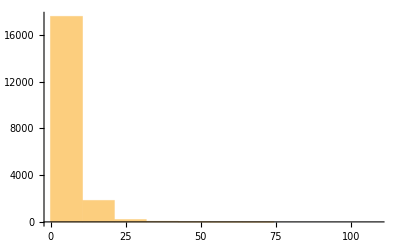

```mathematica
Histogram[words2]
```

#### Basic Classify 1

Validation 10%, Test 20%, Train 70%

```mathematica
classification=Classify[<|"Not a question"->normalLines[[1;;6000]],"Question"->questionsWithoutQuestion[[1;;6000]]|>, ValidationSet-><|"Not a question"->normalLines[[11901;;12000]],"Question"->questionsWithoutQuestion[[11901;;12000]]|>,PerformanceGoal->"Quality"]     (*Training set = 23800*)
```

ClassifierFunction[…]

```mathematica
Export["testclassifier.wmlf",classification]
```

```mathematica
testset=<|"Not a question"->normalLines[[83000;;84200]],"Question"->questionsWithoutQuestion[[16001;;17200]]|>;
```

```mathematica
classification["I thought you lost it, didn't you","Probabilities"]
```

<|Not a question→0.996299,Question→0.00370052|>

```mathematica
ClassifierInformation[classification]
```

```mathematica
cm=ClassifierMeasurements[classification,testset,"Precision"]
```

<|Not a question→0.659649,Question→0.643933|>

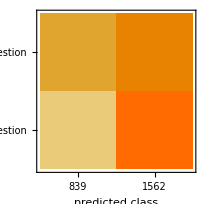

```mathematica
cm["ConfusionMatrixPlot"]
```

If it is a question it is easier for this model to classify it, and if it is not, then it is harder to decide if Not a question is not a question. It says more often that a Not a question is a question.
Why regular sentence is harder to classify as a regular sentence? What kind of text analysis I can do?
It classifies a regular sentence as a question.
Maybe it is because in my data set I have more question than sentences?

#### Basic Classify 2

Removed sentences in questions because some lines contained both questions and sentences.

```mathematica
classification1=Classify[<|"Not a question"->trainnonquestions,"Question"->trainquestions|>, ValidationSet-><|"Not a question"->,"Question"->|>,PerformanceGoal->"Quality"]
```

```mathematica
testset=<|"Not a question"->normalLines[[83000;;84200]],"Question"->questionsWithoutQuestion[[16001;;17200]]|>
```

```mathematica
ClassifierInformation[classification1]
```

```mathematica
cm1=ClassifierMeasurements[classification,testset,"Precision"]
```

```mathematica
cm1["ConfusionMatrixPlot"]
```

#### Basic Classify 3

Removed sentences in questions because some lines contained both questions and sentences. Training Set: 13757, Test: 3650

```mathematica
classification1=Classify[<|"Not a question"->trainnonquestions,"Question"->trainquestions|>, ValidationSet-><|"Not a question"->validationnonq,"Question"->validationq|>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
testset=<|"Not a question"->testnonq,"Question"->testq|>
```

<|Not a question→{Mrs. Mathews your daughter is dead.,Actor who plays you will want to die like hero.,I'm two hours from a Beta version.,Some fool gave the order to distribute rotten food.,Sorry Miss.,By 18-hundred he was gone.,But don't waste time opening and closing hatches.,Because I don't do that anymore.,Of course she might have run away--if she knew how.,These adults are tough enough I think you'll be surprised -- the Mexican's a bit of a question mark -- It's been the same fuckin' thing for thirty years Burt -- ooohhhhhh no.,All this because of that whore!,Go on!,Check the Core for radiation.,I think that'll follow nicely.,Cole I want to get to the farm make sure Little Jim and the girls are okay. ...,Listen my darling...,He has nothing to say.,I done that before and it got me in worse trouble than you could know but I can't stay here no more.,You're dismissed Private.,-- there's nothing to explain.,We were throwing money at him.,Yeah and there's no business as expensive.,I know what I look like.,I don't know you're not supposed to see them.,My faith is gone.,I was trying to pay you a compliment I was guising it as science 'cause I know you're comfortable in that arena.,Sure you probably stick it in tween her knees and think youse there.,Yes I guess it was one 'cause..,In moments of extreme desperation you might even call me sir.,Here's a wow.,' I'm sorry Frances.,O that she knew she were!,I think about what I'm doing all the time and I've got as much business behind the wheel of an automobile as anybody.,Oh man I'm sorry.,He has a mind like a mechanical brain and the more information you feed it...,Have a seat.,Breathe deep -- Keep ya chin down!!,Ballast.,One day you will not be able to come running to us.,One week to graduation.,And it's this place.,If you're making fun of me I don't like it.,I remember it matched the wallpaper.,But even if I were not a priest I could tell your heart has a secret weight and it is hurting you to carry it alone.,I'm really proud of you Frances.,And think...,It's in a safe deposit box, in the city..,There's another thing I've been thinking about.,You told me that on Parents' Weekend.,You are murderer.,Me imanetaba oum dalat!,that which we call a rose By any other word would smell as sweet; So Romeo would were he not Romeo call'd Retain that dear perfection which he owes Without that title.,Oh yes - I just made you Secretary of War.,Come here!,You can't go around pinning crimes on people just because they.97 Maybe.,Cider don't have no taste till later in October--it's too watery now when we're usin' just them early Macs and them Gravensteins.,You know what's happening.,What do you mean I don't understand.,Still..,If I'm not out in a half hour send for the paramedics.,Come on I doubt the answer's that simple.,And  very naďve!,I got it on before this --  -- all started. ...I know what you mean.,Mary Crane's the real name but she might've registered..,You don't think it's too gaudy do you.,And here you are so high and mighty like you're so different from the rest of us.,Luther took a taxi to the hotel across the street.,Bad plan.,it affects you.,Yeah she said it wasn't any use talking anymore.,We're gonna call Domino's and have'm deliver a bigass pizza.,Or at least he used to.,They've turned off the ventilation system.,I just wish it was that simple.,Oh here they are.,My dear young man don't take it too hard.,Green Berets out of Fort Bragg.,Maybe you saw Mary!,Let's go out!,Oh well he must be a surfer.,It's conceivable they might keep something from us but they'd never keep anything from Hal.,I don't watch as much television as you.,Three.,That's what holds us together.,Selena I've been thinking.,Quit acting like some retard or I'll call your mother and tell her what a naughty little shit you've been.,But the variety of food here is very pleasing..,Maybe that's because my the muscles in my arms still hurt.,Ted I think Billy should stay with you..,I've studied the case file, have you...,Impossible to calculate.,And I thought you said it was something special..,I'm not a whore.,Maybe if I can figure out how the memories of a simple worm function it'll help me understand the complexities of the human brain.,Hysterics have a way of severely depleting one's blood sugar, you know.,You're all over the place and whether you wanted it or not the feminists are sizing you up for that poster.,Let them think it was a normal  And perhaps it was .97- perhaps it was.,Well where Mr Carroll uses the word 'love' I look for a new word.,Tell him he can keep them.,We let him pretend he's calling the shots and while he's busy setting up the plan you have time to woo Bianca.,Goodbye Rick.,I didn't see those on any of the other girls..,It spits out on the backside of that hill down the way.,Miles we need papers corporate insurance..,I managed to contact the Mondoshawan.,It's not as expensive as you'd think.,Those guys are world- class warriors.,Greer and Goble in the Call Building San Francisco.,I can't tell from one moment to the next what I'm going to like.,Good-bye Adam.,I am thinking man!,I like your hat.,It's her decision.,Mr. Harris we have fax for you!,But my friends call me 'Bubbles.' Mine's Eleanor.,Mr. Gorman according to our records you have been unemployed for 36 weeks.,Convenient.,No there's only one report to complete.,Full of violence and sex.,Tonight.,You have to understand in Britain in the Sixties you could be a sex symbol and still have bad teeth.,Let's hope he stays that way.,It was first sighted off the French Polynesian Pacific.,I gotta get us a Banker.,I said I don't want you to do this.,Goddam are you suave you fucker.,The Champion is smiling and toying with the man -- trying to give the fans their money's worth and make a show of it with the badly out-classes challenger -- Another left to right combination.,As she glances up at him she is first flustered then flattered then...finally...just realistic:,See you.,Yes boss.,That's very particular.,Okay okay we won't go.,well for a while anyway.,Look it.,She's all I've got.,They live in Malaysia.,Here's to.,-- Go to the bottom.,I have major news to announce.,Bomb must have gone off inside the ship.,We know who the gun belonged to.,Sit down man.,You shut up.,Sorry but it's out of my hands.,But this business got me wonderin' what a good shake and slap would do for her.,I don't want to talk about him.,You aren't talking about money their beady little eyes go dead.,It'll get better now.,Yes you both think William Bloom is a very smart man.,Not what.,When you start your band.,Alright Jeffrey just a minute.,They just appeared out of nowhere.,Left!,He had something.,We are falling back on all fronts.,Cadets Raymond Dunbar and Levi Kendall -- Three things.,Army'd pay for school.,Listen go back and tell the boys to stall as much as possible.,That's impossible.,We're in too far.,From basketball.,In 1935 you ran guns to Ethiopia.,We can live there quite happily for some time.,If you don't want my film - I'll call another show.,Like a surgeon or a concert pianist.,I've seen one of these before.,Fuck you too.,I'll get square with your boss.,My mobile number is...,Shutup you might learn somethin' you're not careful..,I'm here to offer you a job.,Hello Daddy.,And she looked up to him and worshipped him with a feeling she supposed was love.,Shit Principal Cole you ain't gonna believe what else.,And I used to know you personal way back when.,Give them a little while longer.,But I'm the physician in charge and I must do what I think best.,So we go to the bar.,It tells us that he was the last to die.,Hey I ain't cryin'...,King Tut's tomb....,I know I have a tendency to get involved with unavailable men and..,Count it out the back.,Like my pistola.,I mean it's a chemical and all but it works...,I find it hard to tell with you.,Shut up you zombie!,The gravity waves the hallucination all part of an defensive reaction like an immune system..,He's worth a lot more than that.,Only a couple of 'em held out--this man John Horse and his friend Wild Cat and a fella name of Osceola.,But unfortunately for yours truly that train has sailed.,I am a footnote in that story.,It's midnight Harry.,A negative.,Spanish please.,There's a man who throws the ball -- to a man who has a bat.,We need a man who understands dogs -- and that's where this country is going to.,C'mon we're gonna call her before she leaves.,He called this morning from Tuscarora.,Mother...,I was sorry to hear about your father.,But he's not responsible for what happened to the ship.,Our entertainment is enough.,For sure.,Apipoussan!,Sounds respectable.,They say we got to turn around and come right back.,It's all true.,Which anyone coulda taken out of my gear on the chopper.,But also your ring.,You are in a hurry!,We have to go back for Daddy!,COME IN PROTECTOR..,Get on it right away.,Here is my letter.,That's not funny Claudia.,And I say that this FILTH is directly related to this vandalism.,No one in Guilder knows what we've done.,Working on the job.,But you tell me you had a pleasant visit and your mother says you were sullen and uncommunicative.,Well if Peter here would hop off his laurels long enough to marry you...,I figured I better find out who I'm dealing with in case you were looking to hurt me.,That's all I ask -- just two hours to sleep before tomorrow.,I take out the garbage.,Maybe they already have.,Your guess is as good as mine.,Screw that.,The very fact that this choice exists..,I'll call the coroner.,I swear to God!,In a small way.,...with my trusty umbrella.,Well you see the old chap is pretty anxious to open on schedule.,I'll read your report I'll discuss it with the others.,Bailey won't stop drinking and Sarah can't take it anymore.,They should just drop the pretense and name the schools after 'em.,Well I'd love to hear some.,Oh for Chrissakes Amber the woman clung to your tap shoes while flyin' through the air like a Goddamn lawn dart!,And it's drawn to you.,Test of manhood.,Up there.,Pinkerton.,Bobby laid his own tracks.,In about five minutes.,A lot of guys like me.,Well then we should make some effort to acquire him.,We're getting out of here just in time.,You don't have to be sorry.,how unique a people you humans are.,I think we both can.,I can't do that.,I have rights!,Of course it counts.,I want this thing to go to court but my lawyer's telling me to settle.,The only time you come up here when something is wrong.,Fine Lloyd.,Some of the prisoners are easily disturbed.,All the more reason for us to continue his work with the poor!,Hears the FAINT DISTANT RUMBLE OF THE TANK.,Don't look so freaked.,C'mon Max.  First I watch you dive headfirst out the window fifteen stories up like you're Rocky the flying squirrel.,Well it's pretty clear that the front entrance caved in when the bomb went off.,and you're here...,But Sheriff Wade he could shut you down anytime.,We have a perfect relationship.,I mean mouthing off to your teachers.,Just-they're-Huey's too...,A kind of weather bomb.,there's something I'm supposed to do.,There's a Free French garrison over at Brazzaville.,You could still help me do that.,You know Roberta Sparrow.,I've paid the rent the Con-Ed and the phone bill so you don't have to worry about them.,Oh Dewey I'm sorry.,So during those long voyages months at a time out to sea no women in sight a hundred hardworking robust young men in the prime of their life at the peak of their natural appetites desires their god- given hormonal <u>instincts</u>..,Looking for you.,Y...,Please Jam we're trying to vent some hostility here.,I saw you waiting there by the gate.,Drink up young man.,That's got to smart a bit.,But not one women is hunting him - except me.,There weren't.,That doesn't sound -- My writing career!,Ed...,Mrs. Peel had a narrow escape.,Bad enough for--  That wasn't why I called you.,No but there are four guys back there you might check out.,You're gonna die Johnny.,Bus station.,Welcome to Beverly Hills.,Hot Slots that sounds heavy.,I'm Clementine.,This is Basil Exposition Chief of British Intelligence.,A grey lot.,I stole them.,Go on whatcha gotta lose yo' here now..,Ya gotta be a little soft to wanna be a pug..,You should work for yourself.,Couple minutes later phosphorous grenade pops off about a third of a click away -- Oh come on -- Mueller.,I see.,Your buddies this morning went through the mug book but couldn't make a facial match.,It's them.,I'm sorry but they turned down your card.,So I fled.,You just have to be patient.,Vivian I've thought about this a lot.,Looking lovely as always. ...art sank sun set ark sank again...,You ought to be ashamed of yourself astin' such a nasty things a child your age!,Your voice -- it's so familiar ...,I want to document my trip to America.,You'll know presently.,They want you back!,Kid's on Prozac.,I noticed you talking to yourself.,Aye.,That's fine Mr. Rielly but if anyone else should die I'm going to have to get a warrant.,Trust.,Getting the shit kicked out of me by Mexicans.,She is well.,They try and spook each other out talking about zombies and things..,Sometimes if a girl retires she'll even sell it worth good money.,Oh man!,Of course you are.,Of course not.,One thing at a time let's keep him breathing.,You better get back there and monitor the regulatory unit.,Killed two guards and got as far as the Genetic Sector before he got fried going through an electro- field.,Sling.,Right away.,Blow the goddamn hatch!,Tut tut!,But it's a responsibility being a Berserk.,God damit David please believe me!,Just like I guess there are a lot of things Joanna wishes she could change..,It looks to me like we're all that's left of our group.,BASTARDS! Come back here and face me!,That's the way I've always wanted it to be Elaine.,And like in a game of chess you've played every possible move in your head...,Ah yes.,I mean what are you guys..,Anyway stay ballsy.,Hang tough Lloyd.,This is <U>two million</U> Archie.,the crew is confined to the ship when we land at Clavius.,You know that!,Give me the god damn mirror!,Your dried cum.,Simon I didn't want it to end like this.,St. Petersburg.,We're conferencing in Sophy.,U.S. History.,You really are a very beautiful girl.,I will don't worry.,To keep the daylight out!,So he could have gone out to the base hopped the fence dug down into the dirt on the old rifle range and had a heart attack.,If you wanted to you could..,But only cause you're paying me to.,If that happens - It's up to you.,Then perhaps I believe in evil after all.,I knew no one.,There is one other thing..,That Trans-Am was fun to drive.,My mom and I had to change our names and stuff.,I got my mind made up and I ain't gonna be moved on this.,I saw it.,I know you feel awful but don't cry honey nobody's perfect.,Listen Vanessa I'm a swinger..,I used to do it in college and I had this urge to go do it again so I got Patrick and we drove all night to get there and he was sweet and said nice things to me but I was really disappointment to be there with him.,More food the best land for your soldiers to camp.,Well after a few years we got sort of impatient.,I was lookin' for Marvin Acme's will.,Maybe he got killed in the war!,Binding you.,Ain't been right since I moved into that drafty house.,She will be at the ball.,Heh heh heh heh, same old Buddy, always jokin' around.,Hello there.,Therefore she's not immoral.,Go ahead you better leave now.,My mother would have a heart attack.,Hey I was just trying to ...,I'm Sheriff Deeds-- That's me.,We don't even get cable TV.,I could force you.,He fought his way through the trap and carried her body to a secret place!,Well the first month it's great.,Well I haven't heard anything about the disappearance or anything...,I can't go any further..,You must have been crazy.,new is going on here.,But I'II tell you this:,Yeah I worry a lot.,Best known for the tragedy and blood genre this author-playwright -- Willa Cather.,Today Wall Street.,You might as well let him go now.,It was easy.,Face it.,It was the same when I was carrying Will.,I thought a torn ACL was ten to twelve.,I know what it meant to you.,How...,Thanks for your time.,I wouldn't be caught dead in that.,In a very quiet voice.,We never did this kinda shit before.,Good idea!,He was in the bank yesterday.,He said 'Jack'.,I don t think I can...control myself.,You look good Jeffrey.,Our father Montcalm is greater than the Yengeese in the arts of war.,You look like Mush Mouth from Fat Albert.,Here's the data on the Clyde deal.,Trust me you're the best.,Clark Kent if you had only seen it the way I did you - Oh sure.,And as it turns out the Countess is not going to be the vegetable the doctors thought he was..,A fine!,I merely posed a little academic accounting theory.,Nothing's real.,Walk away Jack.,No please!,Oh anywhere downtown.,I think it's Hawkins.,WALKER TALCOTT TALCOTT LT.,On the day he died he was setting a test.,Shhh!,Habeas Corpus -- no bodies no crime and Nunez still plays as self defense.,Those men had a flight last night because of some female in this house and it wasn't Dolly or Mrs. Hillyer.,You're goin' up an' don't care enough to throw Paulie some crumbs!,I'd like a dry Martini.,They're so boring.,The Gods are asleep Erik.,I was able to do her a small favor.,Except for Small Eyes.,Different thing.,It gets frozen this time of year.,I'm thinking.,Just play a part.,He left yesterday on the night train.,there's a salon here in the hotel.,Don't mess with me.,The North Pole is the positive end of the biggest magnet of all - the Earth itself!,U.S. 125 caliber ammunition in it.,And now I have to get back to the news.,Very big specimens -- I mean huge mothers -- and white as snow to coin a phrase except for black tips on their wings and tail feathers and bright red heads.,There's something else I would like you to help me with.,It'll just be social.,Regent Beverly Wilshire.,Most a these guys can't keep a job.,Oh yes you will..,C'mon guys settle down -- Ok.,Just haven't been this close to Toontown for awhile.,I'm Quiz Kid Donnie Smith from the tv -- Nothing special just a spoke in the wheel.,The last is true; the sweeter rest was mine.,HE GOT CAUGHT!,Go to your hotel.,Yeah I noticed..,Those were perfectly good fries Hamilton.,I'm dreaming. ...I wouldn't know.,Secret recipe.,CONTINUED Well I suppose they've been having a bit of trouble with some of the equipment.,I can't leave now.,I'll go along with all you say about me.,Camp Crystal Lake has a full drama program.,Whatever he told me about Bill is just as good now as it was before.,Without havin' good people around ya won't have such a good chance.,It's a new subterranean warhead delivery system.,It wasn't me; you have my word.,I don't know like something's driving you.,She's in bad shape.,And I always knew I could count on you Agent Utah.,Her name is Gretchen.,Look you want to be gentle with that woman if she ever calls again.,It's not your fault it's her fault!,I can't keep my eyes off you.,The only thing which exists is myself.,I realize this is Detroit but I personally find what that rock and roll band is all about to be boring as Lucifer's kingdom.,All the oil!,Yeah, it took her a while to grow up and find Mr. Right, but she did it.,That man followed me last night-- he came from him of course.,This is a fucking nightmare.,Girls decide how far to let you go in the first five minutes.,Jeffrey when you see your father.,I hope you're not buying into this banzai-bullshit like the rest of Bodhi's moonies.,I don't really get it...,It's not like I can't go out and have fun with my friends.,Purely personal.,No way Mister Beck!,Oh no I would have done that.,It's a good one all right.,Let's go eat!,But not if you say so.,All the time 'land land land.' So it's six hundred feet below Park Avenue It's still a Park Avenue address.,We're in the desert.,Goodbye Donald.,I'll give it a place of honor here next to my mother.,No-- They don't hand those medals out for hidin'in your foxhole.,An Irishman is always logical.,Yeah I see her.,Captain Steubing thinks you might work for the police.,We will.,See that's why you ain't getting recruited.,You're honest.,I know how it is to be lonely.,We would settle today for the very fair amount of one million five hundred thousand dollars.,Oh yes Jeffrey.,I really do.,Nobody knew me before tonight.,No Mr. Lowery...,I have six new counsellor up there.,Looks like they've been having a hell of a party here Captain.,good morning.,Sometimes you can hear it like a buzzing the things that happen in their heads.,Don't go near that elevator.,Leave me your address and if I find anything I'll get in touch with you.,Well they should filthy beggars they go from port to port.,No no I wouldn't change a thing.,I wish I could tell you I remembered something new but I can't.,Nobody owns nobody especially not kids.,You might say that although I don't think of it as traveling.,I don't think it's gonna matter.,These automated strumpets are the perfect bait for the degenerate Powers.,It's for you.,He liked me.,But because your department can't do an adequate job in detecting the miniscule number at large it's a problem.,Jump twenty feet!,Herr Seebach was a very kind employer.,You're total CQ Bateman.,You could do worse.,Let's all remain calm.,Linda.,Jack it's all over the papers.,That's just wrong it goes against everything we know..,I was just going to tell you that I love you.,Lots of these science guys never leave that place.,Jack was right.,It's his loss.,I loved the atmosphere.,which means this.,Westley's got his strength back.,Twenty-four hours ago we were sitting in the Pogo Lounge of the Beverly Wills Hotel..,But there's only one problem - you want credit but the problem is - I don't share credit.,It means they're on the attack up and down the frontier.,Just some mercenary who goes around talkin' about the law like -- I won't give him a chance to grab another ship -- or to slash another pilot's throat.,All right then an ordinary matter.,Besides darling the owner of the phone might be a beautiful woman and you may never come back.,Like fish he is.,I wonder..,Seems like she could get a date easy enough..,I'd rather just forget about it.,And a case of scotch to a captain in station assignments.,Four weeks or so right around Halloween.,Victor we can't do anything until the research is ready.,I always wanted to be a cop when I was a kid.,If you'll release me ... whatever you ask for ransom ... you'll get it I promise you...,Marriage bites!,They're part of the team.,Te...,There is a name a term for your kind the likes of you.,It's boring!,I *did* like it.,You don't have any authority-- <u>Jack</u>!,Don't you know you should never let them see you sweat.,I'm going to find a place where I can tilt the field in my favor.,My American Express..,<u>Nothing's</u> real.,This has been quite a night.,I didn't count the days.,Please Maya.,I bet I would.,Oh wow I should've known.,And I for one would prefer the latter.,Andy.,No one ever catches her.,Let's run a current check.,You can expect federal and local law enforcement to go only deep enough to satisfy the law then bury it from here on out.,Mother betrayed me.,I don't think I could ever learn to read that shit.,They'd frame him.,You don't know man you don't know what I did!,Watch closely as Bialystock drives the last nail into the coffin.,It's worth a shot.,Listen Sex Ape.  I'm here to stay.,Johnny get to the command center.,Y'all let me know if these steaks are too dry.,Sit down then.,Can you tell her I'll ring her back.,Sometimes I am in luck and then I lay out my money in these trinkets you see.,I didn't think anyone would get it.,The majority.,Rats!,What's going on.,All you can do is fine him a few thousand francs and give him thirty days.,And as far as I'm concerned he wife and kid are a hell of a lot better off without him.,On most boats a certain loyalty exists between the Exec and his Navigation and Firing Officer.,It's YOU Loki!,Get into their head.,I really shouldn't have -- A religion instructor at Columbia.,And I wouldn't be surprised if he's arrogant enough to think..,You're such a ball-breaker sometimes.,Nobody taught me.,Yah -- I brought her some flowers this morning.,That will make it even more official.,I expressed an interest...,With pleasure.,Sending men up there is bleeding heart crapola from three thousand miles away.,To dump the fuel you have to close the circuit for the pump.,Don't be superstitious.,So I created a monster who didn't work nearly as well as I might have liked -- you were clearly his better  --  he needed more energy more power.,It's not bad but it's bad enough.,But your patient is legally entitled to it.,You know what I said though.,It's his turn for that just now.,I got one..,Helen's going to be pissed.,Creed is down!!,That's why it doesn't often happen to people who break easily or have sharp edges or who have to be carefully kept.,You're just reading me.,I heard you Joanna.,With a K.,Okay number 23's full.,TWENTY-SIX MINUTES!,We've got to hide our identities.,I really don't have that much of an appetite.,She's in the other room.,I'm sure I must have been a great disappointment to her.,Here in Vienna.,Richmond is not all the way down south.,Tapert.,Please be a little more careful how you talk Mr. Mitchell.,Delbert seems to enter #21 twice.,Another stupid idea of my father's!,King Kong.,The Champ backs off.,'Have to go back over there.,It is alright Father.,Oh Harry..,Well I got the papers on my official up-grading to AGS-19 two weeks before we left.,Rescue mission.,Poor little kid has looked forward for two months to having her Daddy home.,You didn't want me going out with Anglos-- I felt that you could do better for yourself-- You made it pretty damn clear you thought he was nobody.,Then forget that.,I don't care how big the deal is.,Look at me.,Human heads.,Drew I don't remember inviting Zowie in for dinner.,And no mom!,But you were punished.,But tell me.,The Mets.,I'm saying I'm sorry.,And I don't want to be challenging or defeatist here but I have to ask and I would want to clarify something -- something that I understand -- This is how you wanna spend the time then go go go -- you're gonna be surprised at what a waste it is -- The most useless thing in the world is that which is behind me Chapter Three -- It's not like I'm trying to attack you -- Not really.,I was by the magazines I could see his face.,Perhaps not today--perhaps not tomorrow.,Good night Joel.,Open it!,You were a galahad compared to some cops I've known.,Sorry babe.,I'm not talking about does.,It's not that I don't trust you but...,Fine..,And I say...,Bang!,He knew Swann way back.,We're moving through time.,They want you to stand for Sheriff next election.,The date.,I was in here yesterday.,Two heads.,I'd really just like to be alone.,You're hurtin' man!,Give them that.,Foot fetish, shit films, watersports, bondage, spanking, fisting, she- males, hemaphrodites..,I will stay here in Freedonia.,Not bad for a man who hasn't slept in four nights.,Almost the same way.,I like him waiting.,Yes I'm having trouble controlling..,You always could.,It's not gonna happen.,Weather's turning quite nasty.,If I didn't know better I'd say you looked almost happy.,You have a little caffeine in the morning I have a little morphine.,So. Nice to meet you Ma'am.,It always is with Clark.,Don't bullshit me!,I've gotta meet somebody.,I might.,The boys on the board are under a lot of pressure from the boys downtown.,I want you two walking the perimeter.,But you can't prove it!,If you want to come up a minute I'll show you some pictures.,They all were.,My only responsibility is to myself now!,I haven't been invited.,Miller...,He's a mythology professor, he thinks crocs are divine conduits.,I never worked for so little except once and that was a very noble cause.,Johns is leaving you a gun.,That's kind of how it was.,Definitely.,That is not acceptable -- Once the ship is secured we'll bring you on board -- Captain I didn't come out here to sit on your bridge I need to be on that ship...,I was beginning to wonder who this Mr. Penfield was.,And the Argies.,Damone I've got to ask you this favor and I'll never ask you for anything again in this lifetime or any other.,Well he was making love to her.,We're just a little tense right now..,I was reading too.,Dunbar's our guy.,Yeah you did!,You know I just sit here listening and you never let me talk.,Two years of surgery.,You got a deal.,We don't know that.,If I understand what you meant by that.,Hey listen aviator here we are!,-- Merely in the interests of order.,I struggled and finally ran out of air.,Suits used to say that in any con sooner or later someone's going to start asking the right questions.,That computer is running this ship and we're heading right for the sun.,Now drop the goddamn gun.,A verdict and premiere all on the same day.,I gotta drop a dime.,Chief - I know I screwed up - but this guy was no innocent civilian.,They come here.,You have to try..,Now try to remember if this girl..,Guess some people forgot their lines.,You were the one who believed in it -- I'm not even going to dignify that -- You poisoned him Bill.,I can accept that.,This is a nice place.,Remember I killed your buddy.,I need real help.,I pay good money only to be taken on some wild goose chase!,Pull me down a bottle of Jack Daniels.,Some tap dancing some singing.,There was only one, but he's out of town and leave no forwardin' address.,Italians are musical idiots and you want them to judge my music!,It was wrong Henry!,Future Man. You know.,No but I work there--I like it.,Ugly habit biting your nails.,I'm not screwing around.,Your a clerk in a rather dowdy Office.,I have always asked for plain information.,Swimming is good.,You're lazy -- That's me Clifford.,Frightening thought.,It was incredible.,Criminals.,We're here to make money all of us.,I walked out on him when he was trying to ask me to marry him!!,You're grounded buddy.,Till I found out I was wrong.,For a change.,Oh you know...,All they want to see is your work.,I know it's not proper to be so familiar but I guess since we're outside the workplace I feel a certain liberty to -- That's lovely.,I gotta use a bad word -- Whore.,I just keep thinking that something awful has happened.,Raymond get enough beer for Ben too.,Edward is taking me to some fancy place for dinner.,Hello..,Unhand that woman!,You never disappointed me.,That's fine with me too.,I was only fifteen.,Go hide.,and my mother!,Teach her a lesson.,I would be thrilled.,We did not leave together.,But Richard no I I -- -- Last night we said a great many things.,I'll get him for you Nick.,Dorothy Vallens.,This one's still with the fire department.,He's beyond our help.,Like he meant it.,You lift off in three hours.,We would receive small amounts of it...,We will not be intimidated.,It's like she owns Jill or something.,Now.,But in one respect you are mistaken.,I've been swimming Merv.,My father is dying.,Wealth and family.,I'm sorry but you're...,I have to call his family.,Assassination.,I picked her up off Hollywood Boulevard.,That's the spirit -- fifty-fifty.,We've only just met!,All that I once loved lies in a shallow grave.,You don't know what you're getting into here.,And after awhile it just becomes part of the game.,Oh Christ I didn't kill anybody.,And this is how I'm handling it.,take your word for it.,For the record.,Those are Sarah Lawrence guys Patrick.,Not criticize -- plead.,I can get you the money.,Clockworks.,No one has stopped here in weeks..,He's the public face of the modern Army.,At some point in there I'm gonna rub my nose.,We can set her up in one of these back street motels hang pictures of Jesus all over the room then turn these pigs loose on her...,It's unrelenting a constant challenge to the senses.,Now you know who I am where I live.,You knew where the money was all along and all we had to do was come here and wait.,Let's get outta here.,I'm glad I didn't ask you for Washington Crossing the Delaware.,HAL J.D.,Lead the way!,He created the voices after the fact.,J&B.,Be who you are right now.,But that's OK...,You're to blame.,I can't say more.,He made pork chops out of her.,Oh and Clarice - next time you will tell me why you ran away.,We couldn't see the bad in 'em.,You've got to make a statement.,This is your job.,Then have a drink.,And you call yourself not a doctor!,And you're beautiful..,I'm not working there anymore.,that's when you start praying all the time.,We just won't have the money to keep you in school.,They just landed in the desert.,Another surprise guest.,Homer told me.,Let me take the lead Stephen..,If it didn't mean so much to Dad - proving his depth-explorer - it's the last thing I'd want!,I thought you were giving up that drug shit.,He's a good provider.,Probably not anyway.,If you let him run around till Tuesday he's gonna run right to Ganz and warn him.,Now don't get upset.,Good friends with Mr. Henry.,Everybody say Ho!,This will get him.,Not bad not bad.,Because of your information I alerted internal affairs to check out Detective Gordon.,I'm invoking rights - this man is represented by counsel.,Not just what it bodes for women in the military -- but for your own confirmation as well.,I've got lots of time.,Well Sire I made some inquiries in a routine way.,Nice kid, mature, didn't have much to say, but they got a sense she's a runaway, so all through dinner the doctor's working on her, trying to convince her that at the very least she should pick up a telephone.,I could tell you were sad.,You'll need to get yourself invited for the right weekend.,So much less refined than frizzling them in the chair.,Peerless you're a good son I love you.,Right on the button.,In fact to be very frank Mr. Mitchell I don't think I like you.,We don't make love.,You're causing a major disturbance in my class and on my time.,It is nonetheless a misfortune and you will know it when you love.,He was giving the most brilliant little concert here.,He's landing.,Well I suppose that I'll have to write Sissy out on the road.,There's a tunnel.,Five thousand now, five thousand on delivery.,But I may miss you just a bit.,No Mikhi I wouldn't.,I'm glad I met you.,To the Fleet.,I didn't say fuck him.,You also state that Bright Eyes had two intelligent companions at the time of his capture.,It wasn't until that they sorted through their gear..,See you Tuesday Frank.,Yet we hear you are making an opera from it.,My friend told me I should maybe even get a lawyer.,No I'm not Kaback is honest.,We have to stay inside for the time it take to refit - about twenty-four hours.,You go back to sleep.,About an hour ago.,There's something wrong with this yogurt.,OhmyGod.,Fuck me.,You have the same chance of winning whether you play or not.,Yes well at first we thought that was the explanation but it's been going on for the past ten days.,Raoul was a...,She's good.,Rick hide me.,I mean just on the off chance she doesn't.,He says that...,I am happy to make your acquaintance as a friend.,Okay bye.,We better take him out.,And I can't imagine that Susan hasn't hinted at the kind of life I lead in London.,I'll get a new one with the insurance money.,That's not good in prison.,You nominated him for Spec-Recon just three days after you nominated me.,I don't think I'm quite familiar with that phrase.,Not about this case though - about yourself.,I'll just be here so you know no one's going to hurt you.,We'll bury him in the morning.,That's very kind of you but we're in rather a hurry..,When my name makes them cry in their sleep.,Okay Fireman.,Are you kidding I never miss a party.,A boy who lies through his teeth buys demonic records and smokes the dope just like you.,One of the boys in the stable told Nelly that you've already bought my horse and that it's at Doolan's farm where Mick the groom is breaking it in.,It's easy to learn.,Hi Mr. Maroon.,Finally there were no options left.,For nothing can be ill if she be well.,Well thanks a pile fella.,Kelly.,He's bound to slip up sooner or later.,What's the plan.,He tried to overthrow Regent Taktra.,You're in the last two seconds you don't cut the crap.,She's got a bit of a bug up her ass.,I didn't listen but you warned me.,I saw the globe in the window.,So speak now.,It seems that something has come over you lately:,I want love in my life.,All right furry muff.,Que sera-sera.,And I just liked you so much.,I'm only asking you to look at this Doctor.,Soon after dis my wife gave birth to a son which of course was my father's brother in-law and my uncle for he was the brother of my step-mother.,If she walks down the street like that an army will be following her.,You know me..,Gee thanks Mr. Dickson.97 Helen while you're downtown you might stop in and make reservations for the bridal suite on the Berengaria sailing next week.,You think it's the wrong moment.,He was playing all this great music- I have to find out what it was..,And my mother called to see if Teddy called.,I'm just outta joint when reporters are around -- They take cheap shots an' Paulie knows it.,Happiest guy you ever saw until the day he died.,And there'll be no pain And no more sorrow.,I need the action.,I thought I'd mistaken infatuation for love.,Row!,Life to Death.,Just loading the last of the CO2 scrubbers.,Bloody hell...,I don't understand it but I want you to know that despite our differences I admire you and I always will.,They smell like cabbage.,Immediate dust off on my 'clear' then stay on station.,Shadow.,What I think I have found out.,Pretty much what you'd expect.,have it...and...my sister has it.,Bring him in.,Why you..,Round up your assholes and move 'em up front we're getting chopped to shit.,Krempe has a way of provoking my temper.,I can't stand this place anymore.,But I have promises to keep.,Meet you on the far side.,Never mind with the too bad shit.,You shot Childs and Nunez.,You're making me feel weird.,This one's out of ink.,Sorry I didn't know your father.,I got statistics I can show you I got graphs I can show you.,You could have quite a party all that stuff....,They think I should - They think I should - They think I should - They think I should be king.,The formality of a trial would be too costly for them.,But you can't explode in the bomb bay.,I acted like an ass and I never had a chance to apologize to her.,I apply my personality in a paste.,Damone never comes to school on April 16th.,We ran out without my shoes and the floor.,I'll take some.,Dad says you're late again you butthole!,I didn't have a chance to wrap it.,There's Mr. Jones!,Warren Hubley was in middle management at a refinery..,But that ground looked none too stable and I don't want anyone -- Thought you didn't believe his story.,Piece of fucking cake.,This package was Kuala Lampur.,You were doing fine you'd been courteous and receptive to courtesy you'd established trust with the embarrassing truth about Miggs and now this ham-handed segue into your questionnaire.,Well . . . uh . . . I . . . Wait a minute.,I swear..,There is very little for you to do but I do need your help.,They're trying to scare us that's why -- to make us afraid to move.,I could be . . .,I have to get to Sugai.,Yeah follow us.,Just hold that thought.,I wasn't about to.,I just hope she isn't too much for him.,Resistance is futile.,Macready and Shilts Legal Services.,He's up there PISSING ON ME! As fast as you can.,But remember this it used to be fun.,Wolfi!,It was on a table in there.,Not yet...,It's jail.,She's probably stealing the money to pay for an abortion.,This is my last drink.,I observe that you in one respect are a very fortunate man Monsieur.,I got this internship while I still was at NYU DeLa was impressed with my get up and go and hired me to be his assistant.,Just let me talk for a second.,She'll never know we touched it.,Trying to figure out what possessed me.,Kiss me, Mr. Hillyer!,I guess it lacks a certain style.,Please don't get up.,Even in Berlin.,The manager looks at me.,People always say you gotta get good with Jesus if you want not to go to hell.,If only the car hadn't broken down.,Well if it isn't Detective Jetson.,Ted.,For all we know we're working for different people.,But not to last.,There ya go.,I can't say I do.,Lecter carved up nine people - that we're sure of - and cooked his favorite bits.,Don't address me.,None of that matters now.,You don't feel any sorrier for Ugarte than I do.,I just made an honest mistake.,No ah...,and I'm not young anymore.,You don't know what you're saying.,But I still got it Eddie...,Don't do it. ...please..,It's a ketch Kelly and I had chartered.,All trips are canceled.,He's . . . cold. . .,Fine I'm doing it.,You forget yourself!,Alright we're going out.,But of course there's nothing self- serving in that scenario.,He is right d'Artagnan.,Grow up stop being such a baby.,They just glow as they drift around the universe.,But let's just have one drill.,No I'm dumber than a goddamn slug.,A further impediment is that the Army garrison has been ordered to move on from Liberty.,Plans are for the architects politicians and so forth.,Rose, that scruffy-looking man is out in the yard again.,I suppose.,Miss Mayfield.,I can't explain it now.,Throw down a ladder!,Fuel level 6.03.,I heard enough.,It's getting cold.,This isn't Houston my friend.,I mean I have to conserve my energy.,Yeah we promise.,You and Frank and Cole and even Bob get all these girls because you're good looking and famous.,Don't tell me you're waiting for lightning to strike.,You say you can't find Tom; all right I'll see that you're paid off; the case is closed.,Broke 70 once on the Shaughnessy Heights Course.,I'm never going to see her again.,Answer.,You all are gonna fuckin' die!,Don't tell me down deep he's really not a bad person and you don't want to see him get hurt.,You're talking about the woman I love.,Unfortunately -- Her husband suspected someone very close to the operation.,We want to help...!,Not even hope.,You're nothing!,Well that is to be expected.,He's talked people into doing things they never would have dreamed of.,First thing stay away from the Children's Zoo.,Down the hall on the right.,We invented that.,Luke.,You lie back and rest Rose and I'll give you a report on it.,The drinking is for the pain.,I wish I did but you're out of my league.,Straightest answer your department's given me all week.,that she chopped up a bunch of teenage camp counselors...,I have to hand it to you.,Sorry Newt.,We're looking for him.,I was reassigned.,That is none of our business.,Of course not...,You know it doesn't include the amp.,Oh no Emma.,It's a post all Vienna seeks.,No I'm sorry.,I ain't in ya way.,But he sends his greetings -- and says that I speak for all the Bruces.,The president is Mel Gordon.,Do you uh know..,You have to be a hero because you think she sees you!,Airport's clean.,No way to know how old the body is without some lab work.,Maureen tries her best to detach herself from the movie.,Well as a matter of -- I read your report.,I've come to take you back to the land of the living.,One who doesn't glow in the dark.,Get rid of it.,Somebody'll see.,A fairly common image.,I'll tell you straight I hated it here.,Have I got a proposition for you Superman.,Carryin' on behind my back.,Cocksucker fell asleep.,We're missing the Sig Ep party.,Maybe I'm too far south.,And here I am daddy right back at the start.,I'm sunk.,Could stop us from ever getting on.,You're my mother!,Vitamin deficiency.,Grazie mio caro Wolfgang!,I tell you this station will be operational as planned.,Hey...hey...it's okay!,You fucking bitch don't you LEAVE ME down here DON'T YOU - YOU Catherine.,People must think the same of me -- a quiet dependable person.,Room was registered to a Francis Capra.,This is nothing.,I have a job.,I'd read all your papers on bioethics.,From mistakes we have made.,it' s alright.,You understand that.,And a city man.,You're the person who floated this amnesia story.,the storm -- Reed stop you need to rest your -- I can...,He works for LaRiviere with me.,Maths always was your strong suit.,Got here just in time.,Gimme your lipstick.,Big one.,I've taken care of everything.,No you dumb son of a bitch.,I've been expecting something.,Teddy was furious when he found out I'd taken tranquilizers!,Go downtown and get a license and get married right away!,You gotta be professional.,But we say cousin.,Michelle she -- The king has invited her to come live in the palace.,Come this way!] No puedo ver la orilla!,I just wanted to be extremely clear so that everyone knows what's going on at any given time.,Get the presents and do the lights.,David your dreams will stop.,Yes Doctor.,I can stop it sometimes but mostly I just jump on and ride it out..,Get'chu at that table up yonder.,Fuck it.,This show makes people think and they're laughing at the same time.,It's just that..,Not even me.,Everybody.,I checked the files.,Well that's good.,I've got to get away from here!,Every person counts every package counts that's my point.,We call him Steve.,Sing!,In the microwave.,We're the exactly the same!,Take it from me you never do.,Anyway it keeps my mind off of...,None of this information got to the managing partners.,Finally I had no other choice I had to leave.,Go 'head.,He knows we're onto him!,KATE J.T.,nothing was there...,I want you to have this picture so you won't forget what I look like.,They won't be here till at least noon.,A very big fish.,I'd do anything for you.,It's like listening to someone else's story.,Plus every time I get jammed-up Gary has an inspiration.,You can't prove anything until we find the bodies!,But you gotta score an I.D.,It had an alarm.,Gloria, much as I hate to leave, I'd be crazy to stay here.,It's not normal not reading letters from home.,Use the sliding food carrier no exceptions.,god I actually had to..,You saw him get bit.,Don't turn him over to the uniforms like some punk.,That's not crazy.,Show a little enthusiasm.,Ted Doctor Sandler says you'll be out in a week.,Perhaps I had better stay.,But this is all you'd be working on.,Maybe.,After you Alfonse.,I'm showing it to you now but you'll never see it again.,I thought it was a legitimate business.,Look at this here!,I don't want to know him!,Don't say that Vizzini.,Daddy.,Pretty morning.,Ah love!,David Reynolds I'm the Manager here.,Very nice meeting you Vivian.,A Fender Strat.,Said looks clear.,She was a crossbreed Chinese and Polish.,Nobody telling you to change this move that around.,Joey Bevo said it was important.,I know this is a bad time.,The bank.,You did not hear me Don Colon.,Or rank.,Delacroix wake up brother man.,It's bad.,I'm feelin' dis'!,I'd love to be macho but this is a pants wetter from all angles.,That's three I owe you.,But blood only means what you let it.,There's a forest a burning forest and you know what I have to do!,Like I'm not gonna see her again.,But my penalty.,We're looking for Ann not making a Goddamn movie!,Just what he told your detective.,Wolfi.,Continue.,Ilia trying to get away from all that.,You know such things have happened.,She with a real man now.,This!,The guy who wrote it joined some freakazoid cult in San Luis Obispo.,I ain't playin'.,Stop now!,I want it back.,You're lying!,I need you to guide us from the comm station.,If he's eaten in the area he shouldn't be far away.,One question.,Others are...cover your ears Son and hum.,I love you Don with all my heart.,It's quite..,He's planning a job.,It's not going to effect any ongoing efforts.,This is my business.,James has got some news.,Also heard that you passed on that little job in Libya.,They received the go-ahead to activate the gravity drive.,You saw it on the subway.,You are completely unfair.,We are Russian.,Can...,As man and wife.,I'd better get going!,It's between you and Rodriguez.,They have noble faces.,Push hard 'cos you got to clear the French outpost by dawn.,Mad. So the Count hired you this morning Rudolfo ...,He'll be back any minute now.,Dark blues grays.,When this thing is over I'll take you to Catalina.,I thought maybe you'd like to hear a song.,I'll make one for you.,I'm already on my way out.,He's a good man.,Easy Dad!,But not many people walk away from double pneumonia, Madam, not many.,Oh it's definitely better beyond question.,Ask Pimm.,You guys got sack I'll give you that much.,I find that hard to believe.,NO ONE ELSE.,General Chiang Chin-wu the Chinese representative is en route to Dromo.,Anything else is morbid.,I need you so much Claudette.,That's the building.,You're having one of your famous hemorrhages.,Our little theory from last night just got blown to shit.,No secrets goddammit!,Like I'm one foot in the dirt.,It belongs to Bob's uncle.,I won't disturb anything Mr. Yow I promise.,If they were in stasis I'd get a location but these readings they're all over the ship.,I guess it took the thought of losing her for me to understand that.,Thank ...you.,I'm not using him again for anything.,So you say.,I don't need any new help.,This is meaningless!,But I'm human.,This will always be the ghetto.,Let's book Charlie.,Well I never heard that one.,Farewell...,We have been instructed to refuel your plane.,they're going to come in here and get us man long before..,Don't tell me.,You'll always remember your first time.,I made it go down the toilet.,I don't know Bob.,There's something funny about that shooting.,Hell yeah.,You're not going to..,They want your assurance.,Broad daylight a crowded movie theatre.,Don't be long Ellen.,Days off are worse.,didn't buy me what I wanted for Christmas that year.,If you give them what they want you can get anything.,Good morrow to you both.,Don't just stand there looking at me.,you can only tell it's the right girl if you're sensitive.,Sam I hate having to be with you in a place like this.,Courtney you're going to have the peanut butter soup with smoked duck and mashed squash.,You were partners with him on some Slag -- uh Newcomer real estate thing.,And the little fame the little fuckin' itty bitty fame that I get in this city makes it a lot easier for my job.,Well I'll be...,Are you going to continue with this.,It had to be someone who knows numbers.,Danny I'm touched.,It's a matter of life or death.,We like the same writers.,We was robbed.,If Phillippe is in the Bastille then to the Bastille we will go.,I like to keep it professional that's all.,Your dad was making a movie.,You may dispense with the pleasantries Commander.,Oh she didn't have to go out to work or anything Dad left us with a little something...,Miles..,Correction.,You never were cut out for this Henry.,He filmed his victims.,I don't know what you're talking about man.,Jennifer Desiderio's disappeared.,Well if I go back on my word I'll kill her.,So have you.,Nothin's comin' close to here without trippin' on somethin'.,Personal-Data Transmitters.,He killed them!,It was just a shag Vanessa.,Won't find West either.,I mean you were there.,It was positive.,F-f-fuck you.,But I thought you said that he was rather...,Time to play Spam in the can.,He -- He made me do it -- Jesus!,Hold the pickle!,I've considered that.,Fuck yeah there is!,I smoke more when I'm unhappy.,We've got our orders.,There's nothing to talk about.,He's a Selectman.,Sir Shiv-a-lot.,Calm.,Good seeing you again.,I equivocated.,Then I'll teach her for free.,The Regent is adding men.,No English lord would trust an Irishman!,Don't wanna miss that chopper.,Fourteen light years for a fucking mindless vegetable that looked like a limp balloon and went squawk and let a fart when you touched it.,After that you rode shotgun for the CIA in some place like El Salvador or Afghanistan a real mercenary.,You're even suspicious of him.,He seems pretty good.,I helped you find him.,I think I should go back.,Well here we are back at fucking school again.,This isn't the time -- Seven guys.,But the Scots dragged their dead away.,It got me outta Woodsboro.,Unlock that door.,Clear for pickup.,I'm right enough to stand on my own two feet.,But from the inside now I can actually effect change.,In between all the other things I have to do.,creature.,This is my niece the Princess Elizabeth.,Forget Tonya Randall.,Tell me again.,The way to a torch's heart is through his tools.,Well Flea I appreciate the respect you just showed me.,Till you get back.,Hope the same thing doesn't happen to me.,We don't negotitate.,I don't do charity.,Plans for absorbing the Tibetan army into the People's Army will soon be finalized.,Yeah too bad.,Brian --  -- See ya tonight.,And when she left she never came back.,It's not cheating ...,It's about forty miles from here.,Let's hear what the majority thinks.,Let's go to Donnie's house.,It's all right I forgive you.,Don't talk like that to him!,There're 20 other buildings.,Okay Joey.,he note that will take us to Asgaard...,A sort of tenseness as if you were afraid of something.,The rest of the company is going to Caen and we're going to the goddamned cheese capital of France.,Means ya healin'.,That's when he called me.,You can suck a fuck.,You're standing on it.,Next week we'll be drinking pińa coladas.,Look you can't buy what I know.,Tom let's spend the night here.,You have to bury your own.,All of his advertising announced the opening tonight.,I've been humming it.,fire..,I think so but I've never seen it so acute.,You however are a different matter.,Well that is the damndest outfit I ever saw in my life.,You're Kareem Abdul Jabbar.,He isn't in today.,Yeah I can't believe Liberace was gay.,But there's never any mail.,He was buttering her rolls.,And the only way you're gonna stop anybody with it is to show it to him and while he's laughing you can shove it down his throat.,to anyone.,Yes yes the song.,We're gonna be working together for a while.,Do you realize what I can create with a single strand of Superman's hair!,We're all square now Harry.,Photography teaches you nothing Ann!,We'll reconvene at that intersection..,Confutatis Maledictis.,My father.,You don't mean that.,Sure meet me at the top we'll start the paperwork.,Caviar French cheese ham..,Come gentle night.,Well let's hope for the best darlin'.,It sounds peculiar but I loved every minute of it.,No he is here.,It'll be okay baby I'll hold your hand.,I'm a hired gun same as the rest of you and that's all any of us needs to know about the other.,It is perhaps strange that we both should be in love with the same woman.,You'll see for yourself... and so will your crew.,Start talking or we're out the door.,We are fucking dead.,I don't think I've slept in a year.,I couldn't help you.,I am also offering you the money so we don't have to turn them over because you can borrow.,Oh I almost forgot..,Speaking of which..,Stephen..,-- fuck you.,It's my last few bucks.,I hadn't thought about it.,This interview's over!,That so.,He bested me with steel.,He's already been.,She was ...,Ooooooh-kayyyyyy.,Tell us the story.,I wasn't saying anything.,I'd like to take a crack at that guy.,Me being a teacher and caring about those things is like an embarrassment--like a betrayal.,You see all we need to do is get a better shot at it with weapons that don't rely on heat seeking...,He gently tries to move Miller aside.,Start ripping them out.,Truth is...,The place produces nothing.,Look at her!,It means literally small but intelligent creature.,You can call him Baby-bear he loves that..,When you asked me to teach you something of the Craft.,It's a rule.,We'll find out whether he's telling the truth.,Yeah he thinks he's evolved to a higher plane of existence or something.,Good morning Court Composer.,Alright it's done.,I thought you might know her.,They are worse than ghosts.,Fucking Northern monkeys.,The Bridge is gone.,Everyone of us on this plane is in a desperate situation.,There was no wallet...,We've got to get ready before he gets here.,The sins of the father laid upon the children is Merchant of Venice but borrowed from Exodus 20:5 and win her with gifts if she respects not words is Two Gentleman from Verona.,Not my jurisdiction.,Yes we sat together at Bell's Square.,Thought I'd kill two birds with one stone.,You might have doubted for say five minutes or so Sister.,Thank you God.,Transsexuals are very passive.,He's sick Bytes.,Delhi.,You have no fucking right you bastards!,The -- Wait a minute wait a minute let's talk a deal Superman.,Mozart - They hate my music.,You should see the tramps coming after Quincy.,He's mine!,Me Lex Luthor who figured out how to live in luxury without ever paying one cent in taxes.,It was in him!,I'll be there to hear his worthless neck snap.,It's delicious.,He doesn't know about the Day Care.,Yes it's...,Doubtless you'll let me know what immensely worthwhile or at least *useful* thing it is that you find to do.,The monster appears to be a genetic aberration..,Look at your dildo partner.,Now let's move 35 degrees southwest.,Kincaid and Joey died last night.,Have the body removed from my cabin.,Oh I'll get it.,Stop in the glade just ahead!,You're just scared.,Also I don't like the smell of the sea around here.,And you've wasted yours on this foul monstrosity.,I mean some guys play anyway but they usually get slaughtered.,Stops.,Let's you live in a penthouse on top of the Vancouver Royal.,Mister Welles.,[Balthsasr shakes his head no.] No matter.,Of course you're All aware a king must have an heir some one to pass the family name along will some one tell me where I'd ever get an heir if a king can do no wrong And everything.,Let none remain!,you're gonna break his little chest bones..,No noise no sound no movement nothing!,Hello  Hi Patrick.,One called Magua arrived.,We have found immortality you and I.,I'd like to break away-- Would you like a dessert..,You know what you can do with that!,No I didn't know if you were talking to me so..,Lady I guess I had you pegged wrong.,Grant as you do everything else with treachery.,You never hurt anyone but yourself as far as I know.,She walked.,I'll put my foot down; So shall it be - This is the land of the free.,I really loved the skilful way You beat the other girls To the bride's bouquet.,He was looking out for you.,Lead mine.,Your son-in-law dealt with the dry cleaning franchise during the day saw that woman every night.,Relax.,You're pissed that's all.,I am sure not.,I can't just walk away!,It's more than they thought.,You Scorpios can never take a joke.,I feel like crying...,I got it.,That's crazy.,You could train someone else.,YOU'RE KILLING HIM!,You're gonna be a straight-A student---just kidding thanks for coming.,Loneliness.,You think you know so much.,I don't know I don't know her anymore.,Oh Raoul..,It gets things back together.,Been on the crop.,I meant to call..,Just get in the car Bob.,I need Il Duce.,The police don't take anything for granted.,Everything's going to be all right.,I can't Barry..,I hate hospitals.,It's called a grilled cheese sandwich you dub.,Unless you Whiskey Run.,You're gonna be seeing a lot of me.,Great just great.,He worships me.,Don't go in!,It's all take take take.,I guess not.,The things I do.,Rest William.,Okay I gotta tell you.,Halfdan has come to kill and destroy.,Even respectability.,Chevalier if you will have your money now you must fight for it.,That's all I know.,Can't live with them can't kill them.,Thought I'd stay in.,New card.,But they could be made to serve the Emperor.,My impression was that he's just another blundering American.,He's so dumb sometimes.,By my head here come the Capulets.,No. no. no.,You think I'm an asshole.,Get back in position!,In bed.,I'll die if I can't spend the rest of my life just looking at you holding you in my arms..,But then this thing happened at the tennis club...,I'm taking you back.,In his mind anyway and soon enough in hers.,She was taught to love the life of others...,Yo' said so yoself!,Nah I got the gun.,Cut out this rotten business and act like a lady.,All right Captain Oveur.,get up!,A trained killer.,We have to talk to her.,A wino!,We are going to make an arrest in your cafe.,He's doing it to spite me I tell you and it's got to stop!,Let me hear it before you check out.,Except he wasn't kidding.,We'll start you off with 60 pounds.,Friday.,At his car.,We better go.,He never pays his debts.,Don't need it I'm a cat I've got five lives.,I don't know...,One fifty!,Don't put your hands in your pockets hold your head up always look a man in the eye and all the time I'm hanging on his every word like he's God or something..,Then suddenly a knight on a white horse with his bright colors flying would ride up.,Well as long as people are still having promiscuous sex with many anonymous partners without protection while at the same time experimenting with mind-expanding drugs in a consequence-free environment I'll be sound as a pound.,They're putting themselves in place of this kid's parents and thinking they'd want to hear their girl's okay, even if that's all they hear.,I can't remember.,The Bible.,I wish I had your kids.,I thought you had to be back to the hotel.,I'm not sure I believe.,Believe me it was a most agonizing.,That's almost half a million dollars.,I'll show you the cabin.,Men fight better without women around.,Reed's always right.,The Old Lady by the swamp.,Please tell me your dawg's not trying to rekindle things with my sister.,It's by Pope Alexander.,Monnitoff says I have to write an essay on the greatest invention ever to benefit mankind.,I think maybe I'm sick.,You're not really comprehending any of this.,Half the receipts!,We pleaded with you to keep liquid but you wouldn't listen to us.,No I loved you too much and too fondly; I have always loved you.,She knows how to take care of herself.,He slaved a year before he was done.,People change.,Up there!,Wade's right it's some kind of scientific magnetic thing I can't explain it but I've seen it.,Bloody murderers.,Save that hustle talk to them field ballers you sell crack to.,I've got it here somewhere..,I would hang him!,There's no such thing I can assure you.,Sold. 45 minutes.,Or unprotected sex with someone you didn't know very well any time during the last twelve years.,Oh, yeah we taped the last interview.,Maybe I was kissing someone and he bit me.,I doubt Bourne's in Naples to settle down and raise a family.,She's fucking nine years old!,I know this for a fact.,I just don't want this to be the thing you'd do over.,I hear Mrs. Swann's quite a babe.,I saw my son.,He'll tell me when he gets home.,We'll pin it on him.,DeLa - what's the matter with you.,For the last time -- SURRENDER!,I am no one to be trifled with that is all you ever need know.,I had Mr. Deegan.,If he's really a bully he won't cop to it anyway.,It's what I do for a living.,Dad I'm so sorry.,I want to talk to both you guys about Greta.,You haven't.,Now now Jack--that just ain't right.,Who else..,This operation is under military jurisdiction and Hicks is next in chain of command.,Cool your jets a second.,Victor's medical facility..,You're kidding yourself.,Things are not what they seem.,Find her get her and tell her I want to talk to her Mary.,Here piggy piggy!,Whatever big head.,I forgot that Rose will lie like a child.,I'll call back.,Defiantly Pagan.,Besides..,Bio-readings of indeterminate origin.,That's my motto!,Use the wand!,Jeffrey I don't think you ought to do it.,Eight.,I didn't lie to you.,That's why there's a dead one on the ship.,About ten years ago..,and when the fire department stops coming...,Please honey.,You don't understand!,I have hurt your feelings.,Right there.,He was pretty much dead.,I can't take this for driving you home.,We just stay clear of him.,That guy wasn't yanking you around.,I see your peach fuzz finally grew in.,You can see my predicament.,All right cop.,We gotta talk about this early morning church shit.,I do too!,It didn't used to be that way.,If you stay I think something bad will happen.,Deer shit.,Scraps.,I don't believe I ever was sick.,Let me see. ...an innocent interest and found out that last year Vogue ran a series called 'Mothers and Daughters' Number seven Anne and Susan Barrington.,Imagine mankind exploring new solar systems colonizing new worlds.,Show me your eyes.,You ain't seen nothin' yet.,I'm sorry but..,And Scotland is William Wallace.,They're going to be valuable some day.,It's not a plan.,you're the Gods....,The delivery boy.,That girl she works at the casino -- It will.,I'll keep digging.,To your health Frank.,You'll be yourself again I assure you.,Guys who'll come after her.,My father..,Well we'll let that one go.,I can't believe this, I haven't gotten more than my hand in six weeks and now this shit.,Bialystock has struck a reef.,If not shut up.,I take it black.,No matter where you take me ... there's no greater hunter than Prince Humperdinck.,Yeah I just got a funny feeling.,Jacob.,I had a boyfriend at the time..,This isn't a game.,And you're late!,You better pray..,That's not mine.,He never told me.,But the scoundrel owes me seventy thousand.,I...I seem to have lost my Congressional Medal of Honor somewhere around here.,Except we've already got the keys.,And my father blamed me for her blindness...,It is miraculous.,There's this guy!,I've been chatting to some friends.,I bet she shags like a minx.,I planned that too.,Vamanos!,Watch it.,Nobody's hearing nothing!,No, Rose, he'll help you.,Oh yes the director.,I wish...,I don't even <u>know</u> the guy.,I need them to go to school.,Something is happening . . ..,I've never seen the ocean either.,A ride home.,This Magua led us into it.  ...eighteen killed.,One million dollars Dino.,Not if they're where I think they are.,For your sake I hope you're right.,The place is to be closed.,Then it...  ...then it...emerges.,I won't know till it's finished.,Bummer.,Nobody tells me about this I have to find out I have to go in everybody's gone - I'd say I'd get you one but the guy who made it he's probably dead I don't know.,The Telegraph office.,I know exactly how you feel.,It's you!,I kind of fell in love with her last night.,He won't.,So many children.,Gentlemen the show our show will be satirical.,Not quite yet Mrs. Mothershead.,And that's why I'd like to be able to help you.,Pussy ass soft personnel.,I didn't find what I was looking for.,You're the one in charge Daddy.,Magua was taken as a slave by the Mohawks who fought for the Grey Hair.,I've told you before wearing boards on your shoulders and parading with a stiff spine doesn't auto- matically endow you with back- bone - !,I'll double the Church reward if you bring those punks direct to me. 100 G cash.,They told me I was too old to serve.,For the last time put them on the table.,With only Columbia abstaining.,Good pilgrim you do wrong your hand too much Which mannerly devotion shows in this; For saints have hands that pilgrims' hands do touch And palm to palm is holy palmers' kiss.,Well I'm not!,I should have got rid of you long ago!,Let's have it.,When I came out Mueller and Pike were dead Nunez and Childs were hit and Dunbar was gone.,I thought it was just because he was worried about me but..,And she was pregnant.,He is coming to meet you.,It's John Bonham's birthday.,I'm not blowin' my young career brother or no brother for you or anybody else.,I'll be back in a flash.,That's so tired.,Applejack!,Please don't ask me to go back again.,Things have not yet resolved.,GIVIN' UP THAT SWITCH LIKE A TRAMP! BEHIND MY BACK AND KILL MY BABY...!,I bet you did such a great job.,You stupid son of a bitch!,You didn't tell me that they can be so nice so great...,If he kills you there you're dead for real.,I mean any sign of the recognizable Earl will pretty much go away -- Ok.,I do sir.,That is the reason why your sister remains safely anonymous.,But everybody calls me LSD. Send for Goebbels.,It's been touch-and-go for a week.,How do you do.,Besides my father I mean.,Kay.,It stops now.,May've noticed chains don't work on this guy.,I think they have another fella there to keep it off your chest.,You're poisoning that child's mind.,Anywhere but here.,It wasn't Tom.,I fell out of my bed last night. ...like fried and chicken... ...like grits and butter... ...like macaroni and cheese..,I  don't hate anyone.,No it actually hadn't.,Gosh that's a pretty name.,Hook's on 24..,Your accents changed.,This is Persian if I'm not mistaken.,It's meant to be clinging.,Oh no wait.,It must be wonderful to be so smart.,You keep saying that but you don't tell me how.,That's him!,Ask Simon.,A very popular drink I'm told.,What you think is important--I think is important.,You're damn right it incensed me the miserable bastard.,You keep me busy.,Without a proper request I'm not obliged to do this you understand -- but I'll make an exception on this one occasion.,It makes it faster.,There's no motels around here.,Look I'm just not wearing this arm band.,It's hopeless.,Mantan way too short too tight.,You would like her very much!,If I didn't I wouldn't put you through it.,They just look at me like I'm the baby brother.,This is so patronizing.,-- No -- not Vizzini -- I need the Man in Black -- That leaves twenty for me.,Hey I got a mother.,I am Frau Weber.,I'm going to take out Diane Court again.,I'm coming!,that's enough.,Michael!,Something's happened.,My memory is good on matters like these.,One rag and we get out from under all this.,Ohh-hh, a little.,she had nothing left.,This don't feel right.,If it's all the same to you I'd rather not dish right here in the middle of Crankville.,I warned you Dignan.,This time <u>I'm</u> gonna kick your ass.,I'm workin' on it.,Oogie boogie.,You ain't been through what I been through Candy.,Then let us toast to your fame!,And the descendants of Japeth are these: Obediah Zebulon Hezekiah... ...,I didn't find out about this very important staff meeting until...,Sweet love renew thy force!,We're dead in the water.,I'm going to die in Casablanca.,Oh you!,They took my daughter.,CARRUTHERS  I'll call you.,Western Union must have gotten the names reversed.,When I'm hoofing I mean really doing my thing hitting it nothing compares to that feeling in the world.,They know you're here with me...,And I'd stand there glued to her shoulder from the time I was five years old watching every hand every move studying how she did it.,You're the faggot.,Well I didn't mean to electrocute him.,There was a partial print they tracked it back to Treadstone!,Passion.,Now somethin I'd like you to look at.,you'd send me in on the chopper with King...,You go out..,I want to complain about this man.,-- Gabriela on the other hand had made an enemy of this man Burgel.,A hunting accident.,Stop a minute please.,Two leagues from here.,No Viagra for me don't need no chemicals.,Disappointing.,Stealing pumpkins soaping windows.,Only your body will remain.,What are you making:,She's coming back.,Hold me touch me.,I shagged her.,That's just part of the island.,If I gave you any thought I probably would.,It was just like she described them in her book.,and blew the whistle on you.,If the military are listening they must immediately destroy this building before they can escape.,You think you are on top now.,It's the scientific method.,Two hours a day six days a week.,I do better to sit in the cheap seats with some real football people.,A tortoise.,I thought it over and I decided we're doing it Murray's way.,It's how on-line services push logos they wanna sell you.,'Didn't know I even cared about that stuff.,He's private property.,Always count on old Wade for a good screwing.,I love a good game of Name That Nightie.,I thought you wanted these people to forgive you.,You have a way of provoking his.,I learned your language you have to learn mine!,That tends to happen when you're the boss's daughter.,Life's looking pretty damn good at the moment.,Wilson.,He said - I can smell your cunt.,Excuse me..,Just sweating it out on the sidelines.,Hey I've got a bit of a problem.,My name is Jeffrey Beaumont - I live near you.,Dat dress will cast ya round..,It would kill me if he went through his whole life never understanding me.,Well we're pretty -- You said someone killed them you said you know who you said that.,Now it's my friend.,I told the truth.,I'm not like a Robert Frost lover by any stretch.,That's correct -- outside it, not in it.,What he did tonight was what he told us all along he would do -- be faithful to his King.,But, if you're asking me who do you go to to get illegal shit..,Okay okay okay-- You were trying to have it both ways and you were being completely selfish.,My name's Sophia.,I worry about you so much.,It looks like you've won this fucking round already so lay off a little for Christ's sake.,I'm kind of busy.,And the Sheriff at the time was Big Charley Wade.,I've got to write some of this down.,The young man Herr Salieri recommended to teach our Gertrude.,But I think the Chief knew that his way -- his world -- had come and gone.,Your experiments could have revolutionized our knowledge of global warming -- had they succeeded.,Lives in Norfolk.,My need to engage in homicidal behavior on a massive scale cannot be um corrected but I have no other way to fulfill my needs.,But your voice sounds so familiar.,We can stop.,A trifle simple perhaps but her appeal is undeniable.,Edward...,There had to be other factors.,Okay but don't kill him.,Well then it all seems to be working out for you.,It was a kill squad.,And watch her til 8:00--I've got to edit.,Now I'm the killer.,They just want us to sit tight.,But first you must confront your greatest enemy.,Turn the light on.,Then - exhilarated.,Your sister Mary is a murderess.,Starling - Maybe he lives in this this Belvedere Ohio too!,He's a lot prettier in person though.,Just don't lie to me.,That's horrible!,Great and thanks for your uh time Mr. Bateman.,No he's really evil.,Right in here.,I don't want a million - I just want one.,And this year...,man.,I'm sorry for the screw-up.,I can't do it Artoo.,Take good care of Mrs. Finley Iris.,I'm ridiculous!,I'm in no mood for trouble!,But I do not think that you will accept my help since I am only waiting around to kill you.,These are stock certificates that we bought in your name.,Probably left it in your room.,Oh yes he will.,I'll use the chair here.,If I call the police your price will go down to a minus sign.,So after we kill the creature we'll begin a search for the nest.,If they had to they'd give him this drug that mimics an alcoholic blackout.,You've been over the line and you came back.,I signed-up for the stock option.,I didn't marry him for love Mr. D'Amour.,Then we had a fight this morning.,I mean if we're cutting the crap...,I can explain it pretty easily.,Next Wednesday I grab a grand from Snyder.,Don't play politics with me little darlin'.,You got nuked in the last quarter.,We'll all go crazy...,Stupid kid.,There may be a few more things hidden.,You are going to drive to the frontier.,Masters of our own destiny.,Obviously.,My partners and I are trying to secure start up capital for a small tech company.,And I don't think that was Tom.,A lot of people made plans before the war.,you can't pretend no more on that.,Shooting in all directions.,Dalai Lama.,Stay out of this Elias.,Well you don't know me so...,oh I refuse to speak of disgusting things because they disgust me!,You've been cryogenically frozen for thirty years.,Not without you!!,Leave me alone!,Say what you gotta say but I ain't gonna hear you speak his name to me.,None of us ever saw him again.,Maybe we won't find the Horn Resounding...,But you've gotta help me.,In case of emergency!,Don't let passion overwhelm you Colon.,No no the key the key to the fail- safe lock!,Just me.,And this is mission specialist Dr. William Weir.,I may have seen her I'm not sure..,Then of course there's the 180 G I'm gonna pick up on the Game tonight -- when the Strawberries win!,Bloody fucking hell..,I was wrong!,Yes but we have not much money and traveling is so expensive and difficult.,That's what Dunbar said about Childs to the letter.,I thing maybe I should just give everything away and go live among the poor people.,I mean I've always thought he was.,well you just might get your wish.,Okay but it has to be a small one.,There's your paint can.,Hey I got it!,We left the office together.,She'll probably charge half price for sex from now on.,Clean the pipe poles wipe down the ladders and hang some hose.,He lifted me up and crashed me down.,Milton gave it voice.,No Sally Viznick's a manipulator he's clever he has what I call malignant narcissism.,I'll join the crowd.,Not this one.,Okay but..,His hand quivers slightly as he unclips one of Wades dogtags.,My Bloomingdale's Credit Card...,Henry Clerval.,Here's the guys I was tellin' ya about -- This is Cuff an' Link. ...No thanks.,Wait a minute!,Watch...,He said he'd be over for dinner at eight..,They'll say he's just pretending to be catatonic and he's completely sane.,Have a nice evening Mr. D'Amour.,Very <u>very</u> rare since the tribe's extinct.,Trust me.,The wisdom of old would be mine - A woman's much better than wine!,And that is completely due to you.,For the movie sound.,Never be caught up caught up like Rosaline and thee.,I got no clue where she stays.,A guy went nuts over off of Commonwealth today.,This is my percentage.,You won't find a better place!,Only you would think of that!,Lieutenant Zipp died this morning.,How ya doin' Ronald.,So I've been playing with this Italian club the last three years.,goodbye Sir!,Go party.,Preliminary investigations may already be underway.,Oh all right.,Mr. Newcombe I have made some difficult loans during the past few years at very onerous terms but 18% a year interest seems very stiff indeed.,if anyone sees it is death...,A lot of them didn't think you would.,-- Is there.,Go to a hotel and stay there..,You have to be experienced to do this.,I don't ask because it takes two weeks to get an answer out here and the answer's always 'don't ask.' There's a guy on the horn mom-and-pop survey team.,I never said that.,I'll tell you what I'm going to do.,Don't worry we'll take care of it.,No just one of them is in charge of them going to the job.,I had some work to do.,I forgot about calling for you.,I can live in or out just as you wish.,It's a private matter...,I didn't notice them I suppose I was too nervous.,The last time I heard from her she was living in San Francisco.,You better be careful Seamus before something happens a plastic surgeon can't fix.,Let's drop back an' boot up.,Things.,Actually no.,Maybe he's got severe coping problems about not having a father.,We don't want to just lock him up; we want a conviction we wanted him to do something more.,I regret that I must leave you here m' Lord m' Lady.,I'm not through insulting your father.,So we'll see.,They had their 2000 years.,He could be working her to get to you.,You are a lucky man.,Yo Paulie.,The ride is over.,Trick-riding is what cowgirls have almost always done in rodeos.,Stan it's Chuck..,Hello...,You I could groom.,O I have bought the mansion of love but not possessed and though I am sold not yet enjoyed.,We're going to make it back Grant.,I'm great.,Tell the jury how many people work in that office with you and Mr. Viznick.,Shit you can't mean it!,They might even sit on your wife's chest.,He's going after the nest.,this woman has been into laudanum.,I have to get up early in the morning tomorrow so..,Give it yourself.,Five o'clock.,That's why it's my fault Dan's dead.,You better hurry.,No Jimmy has a point.,You're not really a murderer yet.,Mom look don't say anything.,If you believe in God.,I know...and I'm really sorry.,Okay folks I think we know how this is going to go...,There's only four of them..,That was very nice of you.,Which has kept him alive.,Half-brother to be precise.,Starck..,You're a terrific mother-- Ted I can't..,Yes character.,It was Daddy's dream.,I'm going to make you eat dirt you soap bubble!,I won't be back.,Yikes!,Maybe mine maybe yours.,You are free to open pod bay doors.,Happy Fourth of July.,Apparently he's been ducking him for like a month.,You're the most wonderful person I've ever met.,Boring!,Crocs hang around the food source.,We finally graduated big dude guy!,It doesn't have anything to do with being smart.,You just detach sex from everything..,About the ballet.,Right now!,I quite liked it.,One Jaguar.,I bet that was Twombley.,And if I helped you I'd be committing a crime or so they tell me.,I'm going to follow up on a hunch of my own.,but, uh, maybe I could call you tonight.,That man that was following us last night--he didn't come back this morning.,It was my fault we lost the Power Source.,Maybe I would if I knew when you were coming back.,no-- If there's a way in there must be a way out.,Where..,You haven't hired me yet.,I'm marrying Debbie.,And some beer.,All deserts have water, somewhere.,The ball...,I think I'm entitled to know.,Just before you and I were to leave Paris together.,The only reason I'm letting you be part of this is 'cause you got the helicopter and the radar-- No!!,And believe me word will get out that you're a pro rat.,On you that'd be an improvement.,Invitations.,I am busy inside.,Backup man from the East Bay.,I'm too young to be so sick.,He didn't.,I don't have all the answers but goddamn it I've got some.,I can't find Mr. Right Buddy I can't find him no matter how hard I look all I find is a whole pile of Mr. Wrongs.,My angel!,He's headed towards the eastern most exit.,one..,I'm talking dire.,Alright alright cut it coolio.,I -- it was broken off.,she's...,There you are dead wrong.,Some figure has been added to or subtracted from..,You said it like it was a big joke Bob.,I don't imagine the answer's on those second-rate shoes Clarice.,Down below's Stanley Park.,All of England shudders with the news of renewed rebellion.,Tom this is our case.,You go on.,One night we went to bed..,There it will stay until called for.,I'm not at liberty to tell you that Miss Weathers.,But I know you don't trust me.,He happens to be an old friend of mine.,Not my style Reggie..,We book two shows a month in there.,Go away unless you got my money.,Get me out!,Eighteen hundred.,They're more afraid of you.,Let's take her with us!,Uh yes you do.,Your quarters sir.,By the way that guy who was in here sniffing after you yesterday called twice already.,Maybe they're not tricks.,Oskar good of you to come.,The stars..,It is too early to implement all the clauses of the Seventeen Point Agreement.,Let go...,It's my life.,One of these nights you'll wake up and find a junkie tearing your bedroom apart.,Oh no no she got all over that.,Don Giovannnnnnnni!,Never try to understand a press message.,Buddy you don't realize it but what you're doing isn't nice.,She stole some money.,Victor your scar -- Just find him.,In London those radical ideas could land you in Newgate prison.,I made it with the principal.,Well not this.,Too bulky ...,Thank you Bloom.,Well tell the asshole to shut up.,Nothing personal.,When you're his age you'll still be pissed off about him.,Musta got some primo bondsman.,I don't know how you've reached that conclusion.,Let me worry about your date.,With the whole world crumbling we pick this time to fall in love.,She was gonna get away.,The card's phony.,Sounds like I'll have to.,I can give you my card, if your clients want to call me..,That'll be four fifty.,Well it's very easy.,I've lost number three.,Turbulence is dropping off... 1000 meters..,Domingo's dead.,I've done an' seen everything'.,Not even in the service.,But I won't do it myself.,You are but a boy.,Bye Adam!,We'll just sell another baseball card.,I've been sweating in this little room with T.V.,MAXWELL Now honey--you are here in time to help me and you can-- Sure--I have one little job to accomplish then we can leave together.,He also said we'd avoid that storm in space.,If I don't make it back here by ten..,oh I think it's GMR twelve zero zero.,You can pause rewind or slow down any details you wish.,Let's not jump to conclusions we need a massive amount of evidence before making that leap.,I sure know that.,You fucked us over.,If I don't see you later -- go to my house and find my notebooks -- and destroy them.,Yes of course.,Maybe we can.,Guy cracks walnuts with his asshole.,No you don't understand I saved a mannequin.,All you've done is try to break my spirit try to turn me into you!,How about five hundred.,Christ if I hadn't gotten pregnant with our son I would have never known I even had sex with the prick.,Only around humans.,Nunez.,When I was your age television was called books.,Here I am Father.,We can make this work Adam!,They have this place surrounded.,But suppose you find nothing but a wasteland.,You got the right attitude anyway look we gotta talk.,He has pains.,Victor this is Roger Murdock.,The more he mocked me the deeper I went.,Get you to the kitchen.,Absolutely I'm 100% with you.,Last question.,I'll be fine Dad.,Don't play God with me Aramis I -- You grow fond of him.,It's a matter of respect.,You can wear it.,Come on Bill don't talk to me about how much money's involved.,As for malignancy, I don't think so, it's very unlikely.,Lillian was here.,Ted you're my main man and if I can't depend on you a hundred and ten percent twenty-four hours a day because you're worried about a kid with a runny nose-- I don't know Jim..,Sonofabitch!,Just entering.,In the bookstore.,That's not the way we play the game.,Buddy quit that you're just a child you're not supposed to be interested in such things.,Dr. Evil I want you to meet your son.,This is private property.,He's a homo.,The first to touch it will be the winner.,Her mom remembers her.,It's a good idea good for you good for the town.,Someone stole mine.,She's very beautiful.,Because I have the Power.,What you made was a big brainless pile of horse shit.,I'm Randy.,It's my own idea.,In fact she's fighting like a tiger.,You're a policeman.,I come back here and you're singin' and dancin'.,Senor Colon an experienced captain such as yourself will understand our concern with the crew.,Hey-yo.,The whole time I was shagging her-- I mean really shagging her I mean it was crazy I was like a huge mechanical piston in and out IN and OUT!,As a child.,I suppose you want a cabin.,Book five Deuteronomy chapter seven verse five.,In 1936 you fought in Spain on the Loyalist side.,It is only too possible.,Your boss tried to pull a switch and he got us all fucking pinched!,You're so spoiled.,Everything you create is used to destroy..,the funny.,Aah!,Let's get him in here.,I will meet you but only one way -- if Robert the Bruce is there and puts his hand on my Bible and swears his loyalty to Scotland.,I knew I could con you.,Joe Zack is a good prospect -- Exciting boy.,Overruled.,They were just tasting the berries.,Well I heard you met Herr Mozart.,She never dared get angry or frightened -- but I said things to her -- it was an attack I know it was.,We all try.,Jennifer.,In fact I would understand fully if the subject matter is deemed too risque too controversial.,It was late I know.,I want to ask you a question.,The ultimate expression of evolution it reproduces asexually.,They have to be the biggest tits ever.,You can't begin to know no one can.,I guess so...,Don't blow it just because of this garbage between us.,I know exactly what I am saying.,It's our only chance.,You know what I'm just gonna crash.,Of course something happens.,They're discussing it.,I told my son not to leave it laying around..,Yes it did.,Yeah you goddamn sonofabitch I know you.,Drunk-rolling job.,Anyhow it never works out.,It's just that goddamn rotten stench.,Earth to Andy.,Not for this.,It might pay to reexamine a few of your more primitive notions.,someone whose goals suddenly seem to be YOUR goals..,And now you risk the same fate.,Oh I doubt that's the case.,Now we play ROUND 2.,I suppose we're both old men now.,You know this place will never be the same without you Ricky.,they's just no money fo'a doctor.,It makes them queasy..,The most important thing you can have is an escape route.,I'm good as is.,My fax said have a good fright.,The good news is we haven't got to your car yet.,Think about this.,Andy!,I read the one about the penal colony.,Till you sell your book.,Pick a suit.,Almost five.,what a waste of a life..,But never so real.,Like I just held them far away from me and they did the same to me.,I will find you..,Loosen up Jack.,I guess since I'm not allowed to go out I should obsess over a dead guy too.,You are not my priest Aramis!,I'm explaining to you because you looked nervous.,About half a cup a day.,I wish I could tell you.,It's *Muddy*!,You don't hold back from me.,For God's sake keep a grip on yourself Janet.,The cows had a brand from a farm just five miles out of town.,'Gonna wait outside.,Make your mind up.,There's a little something wrong with it.,I just saw Joe.  He's here.,Try a wrench on that thing.,Well I guess -- that's what he said.,Miggs has been murdered.,You know Johnny.,If it isn't a baby...,Joshua Strader.,I can't see a bloody thing.,I'm growing fond of <u>you</u> and it's liberating to say so.,I just love being a sister. ..harmonica style is okay. ..it's really about family and tradition... ..we only promote safe rubbered sex.,Sure as hell some dope-dealing bomb freak is going to recognize you and put the word out that you're partying with a thousand cops.,We're all here.,It's broken.,Mrs. Teasdale you're the salt of the earth.,Honest it wasn't.,Fill me in.,Take it back.,It's on a thirty second delay..,This man needs help and you need protection from him.,But you'll not use it to make cheap dramatic gesures with.,Yes I don't know what to make of it.,I'm pretty and sort of clever and very well intentioned and dear God I'd tear your heart out!,Weak sister.,Every time.,The pre-entry signal.,-- Nice dog -- Well I'll see ya later.,Mate in five moves.,You can't go now.,International Satellite Systems.,He doesn't mind because he can't sit still.,Fine just fine!,Look - Oh this is good business in your opinion.,Tons and tons.,Guys I'm after are surfers.,But I hate to even think such a thing.,We have a big day on Monday.,I been at this for almost a year.,Alas no.,Stable.,When all this is over we simply must get you out of that suit.,He's comatose.,If you're possessed you can't reveal anything Satan wants hidden.,I couldn't resist them.,I'll kill them for blowing up my railway!,The previews for next week..,But to a guy like you I'm just another two bit hired gun.,It's the French Secret Service.,All so I could have tap lessons and be in the pageant -- the same one you were in.,I don't fuckin' cook.,--  thought about a rocket that carries a nuclear warhead in its nosecone and can strike with an impact of  -- Albert!,That's what it says.,We didn't have we'd lost it until you came to Casablanca.,And tonight..,You and I are going out together.,You're not leaving.,When I went we called it elementary school.,I am starting him on The Machine tonight.,Neither do I!,I m into well murders and executions mostly.,Let's keep it -- It was stupid.,There is great anti-communist feeling in America.,Darlin' I'll take a taxi to the hotel.,I'm just so proud of you.,We better watch him.,Y'know I'm sort of psychic.,Fine.,I understand you came here from Paris at the time of the occupation.,The floss is garotte wire the toothpaste contains plastic explosives and the toothbrush is the detonation device.,According to this the daughter goes up to stay quiet often.,Mafhkin oble groop..,There've been some calls.,Beer.,Just some rich Anglo out on the lake.,Get one of my guys zapped so some fuckface fresh from the World can get his beauty fucking sleep!,They've done a lot of re-building but society at least as we knew it has utterly collapsed.,lover!,God I gotta be ten years younger and you <u>you</u>...,Buttercup is marrying Humperdinck in a little less than half an hour so all we have to do is get in break up the wedding steal the Princess make our escape after I kill Count Rugen.,Thrill me with your wisdom.,It's complicated.,We're making a statement.,When I'm not thinking about Wally.,Diet Coke.,It is a conduit through which the Lord speaks to us.,It's too late Ted.,Just do it somewhere else.,One would think if sentiment wouldn't persuade him money would.,They got it shoved in their back door.,Willie's just a child.,when she peeled off that gown you'll never guess what she was wearing underneath.,Have sex.,I expect to be compensated.,I'm going inside take a look.,Take me where I haven't the courage to take myself.,I'll call your secretary about reservations.,Then you're perfect.,Now whooping cranes in case you didn't know it are noted for their mating dance.,The chief has been hollering for you.,That's why they're all so big - because he needs a lot of skin!,He doesn't speak English.,In the room.,I will speak to you further when I come.,I've seen a lot of people die before.,Time to quit.,Well excuse me brother mother or any other sucker doesn't make any difference they are still fucking guns and they still fire fucking bullets!,Ah Mothershead.,Your word empty makes me laugh.,If you're any friend at all you'll stop talking like that!,I would have tried not to.,Say Chongo perhaps we could use some extra cash for tasty snacks at the KISS concert our weasly friend won't be attending.,You're very attractive my dear.,Booth!,You got to hand it to them.,Listen that's a pentangle a five- pointed star.,We never would have had this conversation.,And funny.,Your insight serves you well.,There is a way.,You always had a safety net.,Of course I might have brought Gregor but he didn't seem like the right candidate -- for this.,They've taken over this town.,Yeah well...,I give you a fucking chance and a chance and over and over over you let me down.,but I wanted you to be that man.,Mexicans.,Well no one would ever suspect it.,I'm very impressed.,That should buy you ten minutes at least.,Seconds.,Just...,It was racially motivated.,Stay calm!,Please sir.,Thanks for telling me.,Hey Brad.,Theories.,Commander Powell this is Doolittle.,It depends on the quality.,To the pain.,And boy I sure better not try nothin' like that with him again he'll fire me.,I'll shoot your dog...,Somebody steals your gun you're supposed to file a report.,Hey let's be fair.,I told you she's just..,She's fine.,Nah not yet.,Mine's not the CEO.,Don't worry I'm not staying here to be a burden.,the whole time..,The queen had twins that night and one of them was sent away in secret!,I -- Because I just am not drunk enough or stoned enough to make that happen right now.,If we could see our destines manifest themselves visually..,They came in dropped all in seconds and then took their time with fag man.,I'll be waiting.,You <u>did</u> you-- I didn't say it like that.,I do mind.,Bench-presses 350 pounds.,Hey  that's...,Well we all have a degree of narcissism Sally but a malignant narcissist is dangerously self-obsessed.,Let me see 'em.,They pump out 150 videos a week.,For the present we'll go on looking for two exit visas.,Now you're in the shit and so's the department.,No I distinctly remember: you walked out my door.,You come!,It's the key that's kept me locked to you all these years.,You better take Powell and Carney with you -- Right at our one-eyed friend!,This is the United States.,They are not the same thing.,Sit there.,That's a long time to be in jail.,As soon as I saw you loved me I was pleased and I gave you every opportunity to fall more in love with me being certain that for my part I would never love you.,Well, actually, we have a little black boy named Her---t who lives in the garage.,A hundred and one I think.,Where you won't have to hide your mother!,They haven't posted anything.,A sheep dog or something.,Not mad but bound more than a mad-man is; Shut up in prison kept without my food Whipp'd and tormented.,He was just doing his job.,They both looked mad enough to kill him...,The Gods are asleep King Arnulf.,I should leave.,Someone has seen her.,medium deal.,I can't believe it.,They're just fuckin' gone!,Daddy people expect me to be there!,I hear Twombley got shot.,My husband...,But I can heat some up for you if you'd like.,This is no game.,Look come inside and talk..,He's a very likeable guy.,have this thing.,That guy-- from her home town showed up.,BETTES CAROL CAROL DR.,They're town property.,I know where you can go.,Get an education.,Charlie don't do anything.,I love you man Alright!,You choose to do something with your life -- that's it that's what you do.,Anybody could commit suicide if he felt low enough.,I must have been *dreaming* of kissing someone.,I'll wait for you here.,Sit down.,An oh-five Tahoe blue with Wyoming tags..,We've got to keep her away from that bastard!,And you didn't.,I guess I'm terribly sorry again Mrs. West.,Tonight is the night.,You start getting excited!,Here's the file.,A laser capable of emitting a beam of pure anti-matter.,No ma'am he just wanted us to quit.,I hope they give him the works.,I wish I was never artificially created in a lab.,I met a girl.,Try to think of nothing Dorothy.,Just because it is the hard way.,HMMMMMMMM!!!!,Send for my car...,I will never doubt again.,This has nothing to do with him.,Speak to me Fucker.,We also own the Franklin mint which makes decorative hand-painted theme plates for collectors.,Leaving was a business decision.,These passages were constructed for the King's security not so you could step from my father's portrait and startle me to death!,Mrs. Peel ...,I said:,It is my duty to see that you stay in Casablanca.,Put together a score sheet.,Look - let me talk to her.,I'll take that as a compliment.,Let go of your hate.,Mr. John Steed please.,They're African-American.,From the gitgo from jump street.,Accept.,Like this.,You fucked up real good.,You invited me.,My life was too weird for her.,I've already got more help than I need.,I was staying in character.,That must've taken some courage.,Jill please it's alright.,I should be alone anyway.,Don't bother me with trifles; after twenty years at last my father's soul will be at peace.,It's getting too cold even for me Nick.,Not only has this inspired resistance from the other farmers the redoubtable Mr. Alan Pinkerton was seriously injured during the incident.,We got to keep looking.,And then she went to bed and left in the morning.,The fucker shot himself.,I'm burning up.,Ya want the bird go out in the alley an' eat the bird -- I want ya outta the house -- Enjoy ya friggin' life..,That will be just about enough!,I know it's a littler late for an apology.,Only the cops got the whole thing on video tape.,They had every entrance to the border covered.,Oh no Mr. Cluett if it's all the same to you I'd rather not wait.,Must have been my cheap-ass answering machine.,Dr. Chilton..,Please forgive me!,I've got a meeting tonight.,I can't talk about it.,Guess I'm more glad to be here than I thought.,as she got older she became more and more of a recluse..,I don't think She's real big on hate.,Go up to her make like you don't know her and send her into the other bedroom.,When I woke up this morning and saw your smile..,The chance to prove myself my skills my work me.,Probably not. ...,He's in a meeting.,Turn.,Desperately random.,Shrimp and fries.,I can't help you Plank.,I owe you since I goofed up this one.,He is a capable man.,But if you're into her...,that was the last one.,nothing more than some sandwiches and a lot of milk but I'd like it if you'd come up to the house and..,The guys is ready to deal now.,I would think so.,He is dead now.,Buster and I are sitting right here beside you.,No. Daddy says Rose is calm as lettuce.,If I'd 'a known we was gonna have to walk all the way to Ramelle I never would 'a volunteered for this here mission.,You mock my pain!,I think he saved my life.,Ladies and gentlemen...,Money is no object.,We had wanted Paul Owen to come.,I guess you have.,Bingo!,You called me Jeffrey.,Never mind all that.,No listen to me.,I have a friend who might be of assistance.,Hey Janet it's Chad.,Punk.,That oughta help you cope with the injustice of the world a little.,Sluggish.,Your friends are dead.,Thou talk'st of nothing.,Are you a rotten liar.,You warned me.,I just take the money.,We all know what the answers are.,What I resent lieutenant is some politician using my base as a test tube for her grand social experiment.,Well I'm carrying three people.,ee good in bad..,You'll never find it in the dark.,That wiring meets all the safety specifications.,He's a little unhappy.,Oh golly oh just what I've always dreamed of dirty phone calls.,You're trying to kidnap what I've rightfully stolen.,Remember Gus.,I'm not married.,I want to be called Fran.,The kids have no winter clothes..,So you see if it wasn't for me me and my friends would be at that KISS concert right now..,But that can be arranged.,Ya medicine still got a few good swallows in it...,Rules are made to be broken.,Don't even try to play it like you ain't a part of all this.,Catch up with us quickly.,Not your work.,I brung you a little basket of goodies.,And my child you are that figure come to life.,It's another day.,We've been over this a hundred times.,We have a complete dossier on you.,You've run out of things to throw Selena.,Jesus Christ I'm gonna have a stroke.,Bodhi this is your wake up call man -- I... am... an...,We're grabbin' a table send over a waitress to take our order.,That was your idea!,Thirty minutes or less.,Bettina Peterson.,I killed a shit-eating dog.,To the killer.,some people even stuff dogs and cats...,The public doesn't have any idea what we do and now you're going to define our image!,No dances just tell me.,We've got her.] Vi a Rosaria arastrado para el corriente--[I saw Rosaria taken away by the current--] Aqui!,Because I'm pissed off.,and work clothes...,For old times' sake.,Or pee in their pants when they see the ocean!,Next time you go on vacation do me a favor let us know where it is.,Mr. Spicoli you're on dangerous ground here.,But whatever happens in your life...,I am looking for a man by the name of Ugarte.,Any man that can write may answer a letter.,Well you tell him ta take it easy with that.,How quickly they grow up.,They're all over the place.,Well..,Bob taught me.,This is my island.,Soon as I finish the job.,I hope you're right.,Feel like the dog's dinner.,Here's one for the books..,I'll postpone the whole thing until tomorrow night.,I'm not there yet.,He came to see Mr. Cluett.,I'm a little worried about the...  ...about how much bleeding is okay.,What with the weather and all.,They were all over the place.,Poppea.,All right it's Plank.,You did great Ichiro.,I'll make some for us.,I know how you won that election Selena.,You have the classical bone structure of the very great beauties...,Why don't you shut up and let her talk!,Dignan it's got an alarm.,Call the White House.,No time.,It's very different when you have to do it with your own hands.,A tax write-off actually.,I can see why you liked her.,Till then fuck you.,My mother's doing quite well thank you very much.,And death.,I mean I can stay a few more minutes.,MOVE!,But as soon as I graduate...,Rick's got an important announcement to make.,Reiben there's a fairly good chance you're not going to die at all.,How much did he tell you he had...,Not the Bay City Rollers!,The main word there the file heading translates as: Treadstone.,You will be taking Sunday off then..,They need help Lil.,I shouldn't have given it to you.,We've got god knows how much of this stinking weed; we've got a shit load of cash; and we've got a . . . traffic warden.,To set the record straight about where he was the other night when he said he was working late.,I'm eccentric.,Well I guess we're not since we don't have dates .,and then Justin appeared and the Core...,Bad.,With you gone we'll make a fortune rearming the world.,Then I'll leave thee.,She probably had sex scheduled for 12:30.,You're just suffering from lack of sleep.,Well I guess she's more around your age..,Well let me tell you how it is...,He couldn't breathe..,Kit gave it to you yesterday cash.,She brought me my fan mail.,Yes I know the equations---I just can't see it in my head.,We had to have financing.,It's always beautiful at this time.,No it's a...,The juice is climbin' every week.,Great minds think alike.,I'm fucking leaving now.,But -- Louis is planning a visit to the Vatican then who knows where after that.,Here your number's 37.,Due north.,I'll try and make it.,He needs me ma'am.,I was just behind her and I didn't even hear that one <u>shut</u> -- not at all.,Oh -- I haven't flown for a long time.,It's just one more crime you'll have to pay for.,that's a long time..,Little bastards.,Then you put a new flatworm in the maze.,This is the first flight they allowed in for more than a week.,it's not him.,We all know what you did Pike.,I don't have the experience.,Here's what you do.,Shut yer fuckin' mouth.,The latch is screwed up.,I'm looking for Mr. Brandon.,Hello Austin this is Basil Exposition from British Intelligence.,Very well.,There are no vital organs where you're working no major muscles or arteries -- you can't kill me.,My friend you are yesterday.,In a blue funk.,have to..,friends.,And I'm the better outlaw.,To not do that that we've maybe done -- before -- ...yeah...,Transparent spiders plastic men - the whole nine yards.,Absolute fuckin' trouble!,Eve tells me you've been living in a bomb shelter most of your life.,The Bruce is not coming William.,Besides I'm not giving him a third of anything not after everything we had to do.,I've spoken to friends of mine and my husband's in Harrisburg in Lancaster and Hershey.,You could say we represent the <u>un</u>official view of a well-ordered society.,You will stand there and you will listen!,Not tonight.,Could work with a new switch.,Vanessa I have something for you.,Just as on your home planet sir.,You got a punk-ass mouth on you kid.,But Thanks ...,Okay Troy!,Well take care chief.,I have a promotion coming to me.,Not since we were kids.,I'm sorry.,I don't mean to burst your bubble Mantan the Marvelous but Sloan is an opportunity.,Don't be a spoilsport.,I would have had to confirm it previously in order for it to be reconfirmed.,Have a lovely Birthday Party tomorrow.,Sure as a kid.,I meant the other way around.,I'll be watching over you.,Let's make this quick then.,They obviously weren't designed for racing.,We've already been inspected.,One book:,He doesn't seem to be swimming.,You heard me Jesse.,They're in the approach corridor.,I've been through this before and much better I might add.,Ohhhhhh...,Of Course I don't hate you.,To tell you the truth -- you did.,I can't swear up and down like I just did.,Senator Martin...,Man's figured the odds...and he can't take a chance.,I got us through the War all right.,Mmmerrick.,at some point...,I wanted to ask you to marry me.,Your friends use the pool too.,Oh for shit's sake Ted you are the most selfish human being I have ever met.,Thus then in brief:,Make room for Homer so's he can enjoy the view.,We'll just drop all your charges then -- He's lying.,Lloyd is doomed.,You look like you're serious about gettin' to your lunch today!,Please don't go.,No action.,You don't look anything like a three- year-old.,If we pull up to a burning building I'll gladly let you go first.,You either do your job or get ethical.,A real pillar of the community.,A lot of Good guys shoot a lot of bad guys and whiz bang zoom happy ending.,This guy's only half cooked.,I'm here tellin' ya to be very smart with this shot.,I envy you guys.,My partner believes that I should build a horror chamber immortalizing the hideous crimes and criminals of London.,But I like my mother.,And I wish I could, but there's no doubt in my mind he killed those men.,Your Dad and Mom riding off into a new life growing old together happy. ...every time you tell that story you stop there.,It will blow over by tomorrow.,Turns out the short and very simple definition of a gentleman or a lady is: someone who always attempts to make the people around him or her feel as comfortable as possible.,I swear I'll shoot you in your sleep.,Neatly said...but to the wrong man.,It's stupid and boring.,Listen fellas Y'know he's got 'til this week's end.,Look doll if I wanted underwear I woulda broken into Frederick's of Hollywood.,Jesus you.92re just as whacked as your son.,I'm so scared..,Here - keep these.,But he is a big boy now and it is time to move on.,I have a date Daddy.,Mr. Beck the contract states that no body can be disposed of without authorization of--- Shut up all of you.,Bag Cavello.,And you're irresponsible.,Two sticks have the power of four sticks.,It has to be found in exactly the right place.,You'll get your money.,I was just...,I guess it was an accident like everybody thinks.,You never told me why you got kicked out of...,This discussion is terminated.,Don't be so glum Hawk.,But Captain Best is already known as a valiant soldier and is famous as a man of fashion in London.,Spirits.,I'll secure the perimeter.,I realize that the men of this fine institution are severely lacking but killing yourself so you can be with William Shakespeare is beyond the scope of normal teenage obsessions.,Well maybe I was a little bit concerned.,This is fifty bucks.,Hello Louis.,The Trail of Tears.,A woman's gun.,You're so romantic..,Relax it's casual.,How kind you are.,Sometimes in some cases it's necessary to take a risk.,Ahhhh my favorite part of the day.,We're on the verge of answers undreamt of...,But mom!,I'm going to go across the street and get you some sherbert.,He told me because he wanted to know if I wanted to go.,And you ate most of your food already too..,He was a boy riding with the most famous outlaws in the West.,You approve!,Just enjoy your stay.,Here I am honey and I'm all yours.,My features.,I want the best.,Six foot one, strongly built, about 190 pounds.,a long shot.,It won't do any good.,She is the center of their lives quite literally the  mother of their society.,That ain't my scene.,I mean it's cool.,Commander Powell is dead.,All of them!,Yes!,Ten days in Fhloston Paradise for two!,Come on Claudette.,It fit so nice he said I could keep it.,We will be proud to assist you!,I'm trying to slash my wrists.,I'm in a hurry too.,Wouldn't obstruct replication but it does give rise to an error in replication so that the newly formed DNA strand carries a mutation and you're got a virus again...,We do it the hard way.,She's the best media consultant in the biz.,Give Albert Einstein here the Nobel Prize.,Everybody!,Righteousness..,That woman wouldn't of said shit if she had a mouthful.,You shot me right in the arm!,Teddy Fraiser and his crew went on vacation in Chicago for it.,I'm gonna build a state for the seducer and the seducee to live vote breath pay takes and party 'till dawn.,You know I'd be lost without a telephone.,Oh come on.,Over the Edge of the World.,Time.,as something to be used or discarded as we advance the boundaries of what is known.,There's no birthday party for me here!,The lady asked us to promise I wouldn't open the door.,I wouldn't have come if I had known that you were here.,Sooner or later that's everybody.,I'll carry him 'till the third.,I just meant stay cool.,You said so go with such disdain.,Oooooh.,Go on . . .,one thing one play or one movie something that was really fine...,But maybe someday.,We would quarrel for a fortnight then we should be friends for a month together sometimes.,We're in the 21st Century.,I'm turning myself in.,That's the secret of happiness.,I thought these things were supposed to be extinct!,Mrs. Christian Tom Welles here.,You said Trask was arranging laboratory work.,Here it comes again ... the sacred job...,I said bullshit to that line about tradition and family legacy.,Shut your hole Slutnik.,They took two million in cash...,I'm upset too Zee but Jesse and Cole know what they're doing.,Cover my ass.,Without leaving the first time.,It's still easier for you to understand suicide isn't it.,They loved it.,You walked out on this academy six years ago.,I have dispatches a message to Fromberge requesting that Raoul be kept far from the fighting.,Oh I know.,My God Alice.,Over there.,Well I flew in the war but that was a long time ago.,I don't care about rocks I care about you.,Break a leg.,But I ate them anyway.,Those things are going to come in here just like they did before man...,I'll walk over to your house.,Oh yeah well look where you came when you were down and out.,He destroyed everything; my life and my ability to live.,I'll show you!,Can't pinpoint it exactly but I'm going down there with a starsuit and try to find it.,a good friend.,Haven't felt it a bit.,Wait wait.,we...,You see the one we want most refuses to cooperate.,When I was finding these goodies in the shed.,PDT'S.,Poached.,You didn't see a thing!,More like a mystery..,Calm down, let's talk..,She deserves better.,In...,The greatest secret of life is who we truly are.,Whatever you say gentlemen.,I'm a friend of Anna Scott's -- and she rang me at home the day before yesterday -- and left a message saying she's staying with you..,got your pink slip and your...,Look for a kind heart.,You see!,Cause when you say can't you ain't a man.,I remember he used to have these two silver .45's with ivory handles and if you weren't quick enough he'd knock you on the head with one of them.,We can still do this!,Being back here.,No thanks Dad.,Love is a child to be pacified with trifles.,Well please excuse us!,So it us all the more painful and confusing to us that so few of you seem capable of living up the the ideals you set for yourselves.,Students confuse teachers patients confuse psychiatrists lovers with confused hearts confuse lovers with clear hearts....,Not to mention on me.,You're fifteen.,I apologize for the short notice Bill but we've had something come up that requires your immediate attention.,We're heading back to Cape Kenneth.,Janet Made me give you the eye And then panic Janet.,That's a nice attention getter.,I have demanded it -- and common priests present themselves!,On guard glancing back.,I'm sorry to have to resort to such methods but we heard about your good luck on he radio and we need the tickets to Fhloston.,A completely successful fabrication of the past the Ploughman's Lunch was.,Whatever it's going on it's still enough to send you on a cooking course.,You're protecting somebody.,We knew very little about each other when we were in love in Paris.,If Tony says this is it then it's it.,I saw a man he was on fire.,I ate his liver with some fava beans and a nice chianti..,Tranq guns down rifles up!,I'm Steve Christy.,They always come around telling me what a crack up you are.,I couldn't.,<u>Ho</u>tel.,That one's filed and sometimes copied to the Gaming Board.,From now on.,Thanks. ...,Logan had her and I saw him fall...then Peter told me to run.,with your own daughter!,It's a combination of plumber's putty and rayophene gum.,I read that with a quantum increase of seven.,I promised her I'd try to help.,And to me it doesn't make sense to go back to the scene of a crime.,Fuck semantics Doc!,But it wasn't easy.,Be somewhere else.,He's a clumsy git.,You're ruining my life'  Because you won't be normal I can't be normal.,He looks so handsome on t.v. What the hell is he doing in Panama.,Pit of your stomach.,You know that big Indian plays it for keeps...,And put your fingerprints on my lens.,We get the warhead and we hold the world ransom...,I hate to turn on this light you Daddy's awake downstairs but I have to take the chance.,You're a shithead!,You look well.,I did go.,No poor young <u>clerk</u> could find himself in such a fix.,Just leave my family alone.,I have to keep their keys.,Don't help me.,Hey you're a good quarter-horse kid but you can't go a route of ground.,Oh now I'm a bad housekeeper!,He's telling the truth up to a point.,You lost your nerve!,But I am a captain.,That's always a good idea!,Wilbur the adopting couple is waiting in your office.,Oh the things I'll do for one extra vote.,You haven't been at work . . . you didn't call the office . . .  you didn't even call me.,I said I wouldn't hurt her.,Kendall's out of surgery.,I really did.,The way she talks for example.,If she hears her kid's voice..,Nothing's happened to her.,'Cause this is the cove he obviously lives in.,I'll whisper some of the main parts of the story to you.,Go to your tent.,Marty's a good man Brian.,Then you don't have a choice.,It's early in the game yet Mr. Rains.,Just say it that's all.,great skin... perfect..,I mean I can see a tree.,Things changed when you quit the gang.,The bastard deserves to die.,That's too bad.,Sometimes I doubt your commitment to Sparkle Motion.,Chink's the guy's name for Christ's sake.,If he was up there in the dark listening he'd know when she came home know when she found Mitchell dead know what she did about it.,He doesn't make copies.,We missed.,Some time.,The person is unknown.,It was an awful shock to me too.,Oh let's not talk about it.,Sure cousin.,In Paris he continued his activities.,Put your pilot on.,I keep thinking it'll go away.,So I chose my dad.,Only you.,I pick who goes!,I don't mean that the way it sounds.,It does the more you know who you are...,I've been listening to the transmission.,Aw what is this..,I mean I'll give you points for style -- just nothin' for smarts.,It was quite good actually.,Been better Dad..,I think I'm going to throw up.,Do not go back to her.,This is Basil Exposition from British Intelligence.,Somebody's buying those videos.,We'll find out when it goes bad.,Nobody knows why.,You didn't give a shit if you got me or not.,But everybody's treating him like this -- valuable object.,A b...,She'll be going to Harvard this fall.,It could make weather!,And he knows it.,I got scared.,You can question everything you can never know anything for sure.,I mean your parents.,Yes'sir.,When she's on her way over to the apartment you give me the heads up.,Not all Tradition is bad Mrs. Peel.,You'll have to watch yourself there.,We want to produce your play.,Why don't you just stay there and you can have it everyday.,You look very good.,You can't come in here.,Then let her get away.,Ss-ai!,and correct they had him stashed in the Appropriation Liaison Office whatever that is.,He was killed today.,We come out free rich and famous!,Shhhh...it's okay.,But that nigger Tehronne.,He ain't gonna make any more of the shit.,He's one of the eraser guys.,Oh Matt you must be mistaken.,O then I see Queen Mab hath been with you.,Yes Jimmy.,You just ended up together.,Suez.,I'm reaching' a point where I'd kill someone for the nicotine on their fingernails.,In other parts of the world I suppose there are other ways.,You've been living the life of the hired gun -- the well paid hired gun I might note.,If they only knew it they're making things worse for themselves.,That sounds personal.,I'm marking the 180 radial for five and ejecting.,It is time to concern yourself with life.,I'm not getting anywhere.,Listen I wanted to...,Humanity's last hope.,I'm stayin'.,It's full of proper German virtues.,I just don't want to go over it any more.,And one day her sister said to me she wanted to move to Paris so I said okay and she said no she wanted to move to Paris with Francois   and she's still married to him.,Thirty-four seconds!,First you're a slob.,I mean the radiation is gone and..,I know how they reward failure.,One hundred and twenty-five thousand and nine months.,Even if we have the tape that wouldn't shut him up!,This bridge is the only way he can follow.,Damn Evan on the D.L.,I... well...,A lady.,I tried that already.,I missed my window.,Finish the job...,The actors.,I said I don't intend to fire her.,Ain't nobody gonna stomp my electric train...,Y'hear that story the gooks is putting chemicals in the grass so's we become 'pacifists' so's we don fight  Where the hell's everybody they'se gettin high that's what - bunch of hopheads they think they special...,I'm taking my medication.,Passion is something one cannot control!,And I left money on the kitchen table.,Bree thinks he may have been the dumper -- that call she had two years ago.,Tell you what we'll wait right here.,You put him in for three murders, the man saved your life -- There's that word again.,North Korean beaches are the best protected most heavily monitored in the world.,Be quiet and get to the exit.,I'm paying attention.,When Joanna--  my ex-wife--when she was talking before about how unhappy she was during our marriage..,Not..,You're saying this only to make me go.,Good thing he doesn't always know what he's got...,Women are all you have on your mind!,Got a cot in the back- people get afraid to go home they can spend the night.,In many ways Bob's Big Boy never left sir.,You know I really wasn't expecting all this.,Irrigated his face with the shot of J and B I'd just poured him.,Look you'll be back in town tomorrow night.,Okay just cut off as much fat as you can as it goes by and the rule of thumb here is...,Simple numbers.,The emergency number is 327-0800.,Hey be nice to it it'll be nice to you.,Ease off the girl.,I'd rather piss glass.,Seventy- five percent of your job is crowd control.,I can't stand it I gotta find out what's going on.,Listen to the animal cracker roar like a lion.,See that's what makes it a joke.,I have no sympathy for either good or evil.,just tap on the wall.,All the posters and newspapers are calling this bunch the James-Younger Gang.,It's hard to know.,Mami the first time I brought him home those were your exact words-- some chulo with grease under his nails.,In my time and nobody else's.,Now we're on the right track..,Greek numbers 600 60 and 6 - or 666.,An old car like this it depends on the condition.,But I will make you happy...,A condom.,I'd rather sit down for this one Elaine.,This is for me.,It's nice.,You do not want a guy like that loose on the streets.,Let's make a note of that.,West is dead.,you're y'know..,my Porsche..,But you can't forgive for Liz.  No one can.,He's been rulin' Toontown ever since.,I think you're a freak.,And he is one smart man.,You will be paid well.,Of course you will sweetheart.,Oh geez I'm full of shit.,Great Mom. I'm using the same caterer for the shower I had for our Christmas party last year.,I want to drive awhile.,Dorothy!,Let me get my purse.,I had nothing to do with that I tell you!,O tedious is this day as the night before some festival to an impatient child that hath new robes and may not wear them.,They wouldn't run..,Please Your Grace give him one more chance.,Tell Mommy that I called.,Until we return to base and ballistics can match your weapon to the slugs in Sergeant West's body -- Bullshit -- You are to be stripped of all weapons and placed under guard -- The fuck are you talking about -- Cadet Michael Mueller I hereby place you under military arrest for the murder of Sergeant Nathan West -- We're not going anywhere.,Joan Gale's body is packed in the box in the basement and I saw the most horrible thing down there.,It's a combination of acetone turpentine and paint remover.,Look at him.,Don't think about it.,They know.,Five total to launch.,Not as long as you insist on living in the past!,Kaminski.,Anytime!,You're getting me hysterical.,Unfortunately not sir.,Good night Alice.,It's 11 I've won.,At least if we don't sleep he can't get us.,My dear it will hardly enhance your reputation to be celebrated throughout Vienna as a singing prostitute for a Turk.,He's done some work with our museum.,I've checked the records of Jane McKenna's death -- I can't get anything special.,It's probably easier for you to eat the rice.,I could go out of town.,And that's the way it happens.,Maybe he didn't know exactly what he was gonna do but he had a pretty good idea.,Right now though I can't.,How great to see you.,We have a visitor.,Opening pod bay doors.,At this time of night.,I'm willing to do anything to prevent this war.,Whattaya say we have dinner then maybe head out to the beach rub some of this tan off each other.,I need the braces.,I could start with your haircut but it doesn't matter.,Okay I got it.,I have felt him my Master.,Enough of that crap.,A fire which never dies.,You are not to detonate repeat you are not to detonate in the bomb bay.,That's what people want you know: fantasy.,That might be the news we've been waiting for.,I know when people is in trouble and you is.,In the fur business.,Now come on tell me.,panic button.,These guys are smart.,There's two thousand dollars unaccounted for.,I made a deal with some minor league Bad Boys.,So...,A French & Indian army out of Fort Carillon's heading south to war against the English.,Bastard's got his high beams on.,You reek of Mrs. Peel's Black Leather ...,I'm not asking you to marry me.,Man you must really hate my guts.,My folks are.,You get it quick.,He recovered from his wound.,Thank you for seeing me.,I don't want him.,Ain't gonna...,I could use some help.,Because I've already found the most wonderful libretto!,This is one time we could sure use Elias.,The king can do to wrong!,You said there was a deal.,But the quantity it does not exist.,I mean it's not.,Quite a compliment coming from you doctor.,Well only one answer can take care of all our questions.,I'm home from school.,Why - er -- my husband passed away..,For no reason!,He will come for me.,You have to stop this!,Well not me personally.,Hey--she's in a tough situation.,You could make your own cinnamon toast.,Wipe that sad-assed look off your face before you get us all busted.,And some others.,Luke don't talk that way.,I thought I told you not to answer the phone.,Gee Uncle Lex I don't think this guy's much of a dancer.,Don't ask me how I know.,The entire state of Texas along with the FBI is looking for you.,Resistance when it is not.,I'm not afraid to die.,Your integrity is unquestioned.,I don't like taking mortgages from widows.,Then go to bed.,One person says something to the other and that's how it starts..,If I've got any sense I'm going to call headquarters.,I guess Ron hasn't called yet.,'Cause guard sounds too weird.,no that can't be right it says three years.,Promise me you won't butt in.,If you're insulted and not satisfied remember there's two of us Best.,Once and for all.,I don't think you will.,Shakespeare was French!,I must be getting old - I thought you two had something going there.,The fuckin' woman the hostage.,Music!,Just what is your position if you don't mind my asking.,It's client.,Excuse me ladies.,just having a laugh that's all.,Whatever somebody does to improve things around here you gotta find fault with it.,They can't erase memories.,Thank you Desmond.,Evan Twombley the union boss who got shot.,Looks like Web Mimms wasn't the only casualty this town's got.,She said it wouldn't last.,In refugees alone we could make a fortune if you would work with me through the black market.,You know how like they say you save someone's life you responsible for them.,Rick there's going to be some excitement here tonight.,They're going crazy.,Over three-hundred.,First there's this one..,You're buying the town.,she's dead.,Couldn't wait.,I can put that together.,No sweetheart it's a stag party.,Hey -- I've gotta have a few clients when I get to Wall Street.,Tear them up.,Mostly regional stuff but he's rumored to have a big tube sock ad coming out.,As long as you're around I'm sure the sun wouldn't dare go out.,I told you before you wouldn't understand.,We had a kid pass out in the men's room.,Maybe it's because I love Debbie or maybe it's hard for me to get off in a place that smells like egg salad.,Let us pass at once!,Good morning Mr. Crawford.,Anyway she was a runaway arrests for vandalism petty theft drugs the whole bit.,But like a gentleman he scorned to apologize.,We will bring him to his knees!,You're dead you're fucking dead Elias!,But they are not ny people.,When you've done that you and I shall give the man a bath.,Don't mention it.,Also I'd report the person who gave it to me to the police.,Well I need to study and...,The papers said the safe door was opened Eddie.,Because I have dreamed of him.,I can still hear it.,You need me Selena.,Good night my dear.,I had to dump the papers in a trashcan.,Imagine--she was alive.,I felt like a Nazi but it had to be done.,You -- You cannot ask me to betray my king!,I just don't want to.,If it worked yes.,You sure talk like a girl who's been married.,You and Mel and Jack.,It's a fucking kick in the head.,Hank!,Not as long as I'm President.,It took six months of research.,You know my son our lord said..,Forty-three days.,Deb it's me.,Why backdrafts.,I wasn't officialy enrolled, that's right.,It's Saturday.,The male was stabbed so hard the killer broke off the tip of the knife in his spine.,Nothing to discuss.,Nadia is my little cousin.,Brutal day.,Just...say...no!,Felt promising.,Young Mitchell's father.,Yes but I'm the only one who knows him.,He wants to meet you and David Van Patten and Tim Price at Harry's for drinks.,I guessed you weren't a stickler for Tradition doctor.,Here a man is made to look a fool for standing out.,Your mother's dead but your father's alive.,And I like him that way.,I love you dad.,Call the skank now or I start redecorating.,You better leave sweetheart.,coming home...,She lives with my parents.,ERIK!,You're making the right decision sir.,You use Evyan skin cream and sometimes you wear L'Air du Temps but not today.,They take you away to San Clemente Island.,Not is Luis a despicable twit.,It's no deal.,Hy-Brasil is sinking!,Thanks for helping us out Ed.,You were with him at the end.,Jack you're not the usual type we get here.,You have great tits.,I worry about them.,I had that fire.,Skipper please..,I never know anymore.,That kiss ...,I'm totally and completely serious.,Okay here's the deal.,This isn't gonna be easy.,I mean for good Jeffrey.,I can try Dad.,To make money.,Applejack was the wheel man.,Smells funny it being mentioned in the paper.,They're looking for the new Tatum.,The only thing that cunt's had behind her is me and half the town fuckin' her.,Many times in damestic abuse situations the young lady is afraid to speak but I have to tell you that being a police officer I've seen it happen: Young woman afraid to speak next thing you know I'm gettin' a call on the radio I got a 422 -- -- is not my boyfriend.,And I'm Gonna Turn Away And Walk Now And Not Look At Him Not See My Man My Earl I'll leave now...and tell him it's ok and I'm ok.,I loved Arlyn I took her right into my apartment my own sweet apartment on First.,And I didn't like what he did with your opera.,I want to go to an East Coast school!,However as regards this witness I'm going to sustain the defense's objection.,Another summer of working at Swenson's.,but she could have been...,It's not far.,You don't have to be polite Clark.,So do I.  But the way it was explained to me that's not the issue.,So far masters of our own demise.,Goodbye's make me crazy.,We're up to our ears in them.,I haven't seen you around here.,I can't marry him he's too young and hasn't got no job but he loves me...,That depends upon your motive.,Ours is not to reason why.,Well dear you see I . . . I . . . Listen dear.,No problem lieutenant.,I finished that.,It's pure hell--if I never see another chicken I'll be happy.,Learning language.,YOU BURN IN BELL.,Now here's how it's gonna be Lydia.,I couldn't pass the test.,This isn't pots and pans this is a precise business.,Oooh Baby you were the best.,as you can see...,Sorry I'm just a little anxious to give it to her.,Better no cowgirls at all than cowgirls compromised.,I had to clean up.,And only you the original Yoni Yum/Dew Girl could possibly assist me.,You're a beautiful woman.,He got my gun!,No I know.,My shit is together.,You make me sick.,I use my cell phone to get computer access to the telecommunications satellite used by our target.,Tell me more..,Even when kings are hunchbacks they have any woman they desire because power seduces even more than love!,Que les bons temps roulČ!,We talked earlier about your mother.,I can't give up looking for her Mrs. Redi no matter what you're hinting at.,I can't sleep.,Playing.,You don't know what it's like out there.,They'll fight like hell if you try to take the head without the dogs.,Crawl faster.,Field of expertise: chemical manufacturing.,You're on.,Never.,And it's all yours for the remarkably low price of only $200!,He stabbed my mom four times in the chest.,And watching.,He drove off without her..,Why it's just one huge nuclear bomb.,If you will be patient maybe I will pay you something another time.,I think you did alright by God under the circumstances.,Thank God your fever broke.,Like she was havin' some kind'a fit.,But don't worry I'm clean as a whistle.,Go on ask them.,I'm really the only one qualified to remote-pilot the ship anyway.,Apparently so.,It's totally disease-free.,It's a farce.,It might have been that broke from 'Fiddler On The Roof' Toppy.,Maybe you got him Hank.,'Course I am -- but doesn't mean I won't leave you here.,And if I'd made it a major security situation the Administration would've stepped in.,We'll meet at the shield generator at 0300.,Liked to talk.,So I pulled a few strings at the State Department...,I have five-hundred dollars.,No No arguments.,Surely you're not suggesting...,Por favor Senorita.,I'd say..,but I can't...,He's doing no harm.,But so many suns have set since Le Renard struck the war post.,more American.,Which would make her termination date..,oh my god..,In our current environment Dr. Weir self-control is an asset.,You know he'd fight a buzz saw for you - he loves you so much.,If you know a way out of this place and you're holding out -- Easy.,How about me getting the help.,Don't be over-dramatic young lady.,We've got to get to Amanda before it's too late.,She could blind me as easily as the night the day.,Uh..thanks.,I'll see to it personally!,Like I'm shocked to hear you say that.,C'mon Larry.,There was a mistake.,Oh but if Jan should find out!,I talked to my ex he'll keep Denny over Christmas and I'll get him this summer.,Could have been buried alive.,I've thought about it and there's no other way.,No he wasn't.,Yes you do!,I'm a grown woman and I can decide about my own life.,Far as I can tell he hasn't even lied to us.,Don't let the bedbugs bite.,Her name is Kimberly Jane Emberg she was just ID'd.,Maybe so.,Women!,Go sit over there.,Of course I'm on it.,Like steel.,No offices are gonna be open today.,Our experts aren't as smart as theirs.,Did you say the last blackout occurred when he was with his friend's dad.,Look we'll talk to the A.D.A. Danny he isn't gonna find out it's you.,I'm fuckin' done.,Sooner or later the truth'll come out.,This isn't homicide school.,Perfect.,God forgive you for how you done me...,I don't know how you could change bedpans sober.,Anyhow...,He has a wife called June.,Through the telephone line terminal that ain't nothin'.,Tower Air Force One has been boarded.,I have something to show you.,I know why you broke up with me in college.,Four digits.,Folks get sick.,En ingles Enrique.,We let you have twenty-five thousand men -- and we both start even.,But I'm taking no chances.,Getting there.,You're a smart boy Jeremiah.,I'm really touched.,Let's go NIGGERS.,I never seen the guy get shot I told you that.,I'm a wanted woman I know ...,The King.,You are the only colleague who did.,We've got to go to the asylum and find her body.,Excuse me I have to change.,I agree Baron.,I just wanted to ask him a few questions that's all.,Yes sir of course sir I was merely speaking hypothetically.,No he's not bothering anyone.,Probably have a copy of my birth certificate...my apartment.,I'm Mary's sister.,We've been expecting you.,They took everything..,That's what my Mom always says..,Nothing unusual.,A common thief.,The money the gear!,I just wanted to see if you were all right.,While I was talking to Frank on the golf course.,SULLIVAN LANDON LANDON REV.,Don't lie to me!!,CAPTAIN IF YOUR MOTHER SAW YOU DO THAT SHE'D BE VERY UPSET! Rolls his eyes takes a breath.,He would have been useful in the fight to preserve the BBC's independence during the Suez crisis - one of the few things he was passionate about.,The eternal nothingness.,Then it's very simple.,Ever since you were little you thought you were too good for anything I had to say.,Oh I don't know.,The Lifeline is divided that way.,You make so many friends.,Mueller went after him but we held him back.,Almost got it.,I almost got my ass blown off twice tonight for nothing.,Get me drunk so I don't stick my foot up yo ass.,I thought you liked Rose.},Question→{You think you're so god damned smart don't you.,Well what's the situation.,And they grow out of our stomachs.,And what was so important about it.,How much did they cost.,What does she sell.,Do you know where we are.,How you holding up.,That phone message wasn't for me was it.,Leaving what.,Who else can I ask around here.,Why don't you ask your chief detective.,L627077 L627075 L627074 L627073 L627072 L627071 L627068 L627067 L627066 L627065 L627041 L627040 L627020 L627019 L627018   * What's the plan.,How did you hurt your hand.,Well what should we do.,Grounded for the rest of the year.,Bad people.,Why do you think they let us in on the deal.,You know how I know.,I know but it wasn't all bad was it.,Lots of people worked for her she had the business from all these retail stores.,The one who was gone for a year.,Have they located my daughter yet.,Which one pulled the trigger.,Then how come they haven't set the bail yet.,-- the brothers.,Where did you learn to shoot.,What the devil.,What deviant groups or organizations did he secretly belong to.,What about my orange juice.,Fight their hearts out for peanuts -- But who cared.,You know what gets old.,Who's next.,Why does she keep repeating the name.,Thelma do you know where I could be in this business if I had a wife that entertained or went out socially-- Did it ever occur to you guys that Joanna Kramer's not the easiest person in the world to live with.,It isn't rape then is it.,But...has anyone seen him in London.,What do I do Dad.,Did you threaten this man or use profanity in any way.,And he is still willing to give you a visa.,Hey do you think you could eat me if you had to.,Max, what is it.,See that patch of shirt.,How do you know this.,Do you have a cross.,Pupils.,Detective - can you tell us what happened here.,Something wrong with the stairs.,I might not be able to see this through.,Are you a punk.,Some kind of virus.,Why loose your venom on me.,Missing..,Any movie stars buried here.,Is she the kid you're gonna save from the burning building.,Shall I be forced to feed you David.,So that's why we can't get along.,And Mademoiselle.,How did you know my father.,He didn't fall.,You mind if I take a swim in your bathtub before I hit it.,Do you have to be so damn forthright.,More than three less than thirty- three--permanently.,Where is Reed.,Are you familiar with the work of Aristotle.,Did we.,Why what do you mean dear.,Rick what's the big announcement.,in that room.,Must I remind you that he is wearing a costume not a uniform....,-- you decided you liked it after all the other night; you'll hang around for seconds.,Have you known her long.,Shall I ask the Chief of Staff to schedule your daughter in.,Stick around please.,To get from here to there.,How long you been working there.,Keep your chin up and your music down alright.,I'm the guy who took the pictures of you and Acme playin' pattycake remember.,When did anyone on that paper give a damn about workers rights.,I made her feel guilty this morning --  Brother what are you doing up.,Shall I send a car.,Will you shut up!.!!,Where is your attacker.,Then why'd we tie him up.,You don't mean to tell me you are living in poverty.,Shouldn't you be in your room Jacob.,Give a guy a break will you.,The Wolf.,Philip Swann.,Isn't Mr. Lowery back from lunch.,And what do the boys on the board know about safety Commissioner.,I do things and I fuck up and I fucked up....forgive me ok.,Is it true the most you've ever made in a prizefight is five hundred dollars.,What did you find out.,Me.  I don't think so.,Whose rooms are those.,Can you accept this mission and keep it private.,Will you kiss me.,How you doing back there.,I can see that what're they for.,May I just do that Majesty.,Do you remember the detonation time.,The grandfather clock.,You'd take no offense if we called you DeLa for short.,Can I help you with the dishes.,How now Balthasar.!,Twenty-five.,What're you trying to prove.,Give me some.,What have you two been doin' to make it look so nice.,what kind of monster client have you picked up this time.,Hey but did we get to you Klute.,Were all these people questioned this afternoon.,Could I borrow your guitar.,New hitman wants to leave his mark And the pennies.,Hello Pinback are you there.,Why what sir.,How did it go.,Mom do you want some time with Dad.,Well what have you got.,In movie they make of us who do you think would act me.,Louis are you pro-Vichy or Free French.,I'm lookin' scared.,I've heard Wade was a bit tough on the Mexicans-- Out in the fresh air nice gringo lady making you pies--who's gonna sit back in a little jail cell all day.,Hi again how's it going.,Listen this is the time when the big boys have to go to work okay Honey.,What did it say.,What did you wish for honey.,Then why didn't you talk to the reporter.,You'll see that he gets out.,Under <u>water</u>.,Relaxed.,So how does it happen.,You don't find that repugnant.,Will you be quiet.,Shall I leave.,You're not allowed to speak remember.,Where's Leeloo.,TELL ME!  What is it.,What changed.,You're going to wait until she's asleep.,Is Detective Gordon going to be at your house.,What do you get out of it.,When will you stop.,About clothing.,Where's Ronnie.,How'd you spell that again.,Now - So they caught up with you too.,Resistance.,See y'later.,Me.  Thelma I'm not hostile.,I'm not a doctor. ...so you feel absolutely no responsibility for killing these people.,What is this Twenty Questions.,What's causing the readings.,Listen why don't we go into the back and shag.,Do I have a choice in this.,Next year if your grades are high enough-- Dad I talked to the track coach-- Dad can I talk to you about track.,Then I'm free to go....,You get nothing Hank okay.,Do they have cable.,How'd you get a tux at the last minute.,What about this week's check.,What if she forgets.,Who determines what is black.,What are we doing.,Do you have the suspect in custody.,East above the river heading for the Eagle Pass.,Projectile diarrhea.,u6569 u6572 u6569 u6572 u6569 u6572 u6569 u6572 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6572 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6570 u6572 u6572 u6570 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6574 u6570 u6574 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6572 u6576 u6572 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6572 u6576 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6572 u6576 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6577 u6572 u6572 u6577 u6577 u6572 u6577 u6572 u6577 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6574 u6572 u6574 u6572 u6572 u6574 u6574 u6572 u6574 u6572 u6574 u6572 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6575 u6572 u6575 u6572 u6575 u6575 u6572 u6575 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6579 u6572 u6579 u6572 u6579 u6572 u6581 u6574 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6575 u6581 u6575 u6581 u6575 u6575 u6581 u6575 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6581 u6575 u6581 u6575 u6575 u6581 u6576 u6578 u6576 u6576 u6578 u6576 u6578 u6578 u6576 u6578 u6576 u6578 u6576 u6578 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6581 u6576 u6581 u6576 u6577 u6581 u6577 u6581 u6577 u6581 u6577 u6577 u6581 u6577 u6581 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6579 u6581 u6579 u6581 u6579 u6579 u6581 u6583 u6582 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6588 u6583 u6588 u6583 u6588 u6583 u6588 u6583 u6589 u6583 u6589 u6583 u6583 u6589 u6583 u6589 u6583 u6589 u6583 u6589 u6589 u6583 u6589 u6589 u6583 u6589 u6583 u6583 u6589 u6589 u6583 u6589 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6583 u6587 u6590 u6583 u6590 u6583 u6590 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6583 u6590 u6590 u6583 u6590 u6585 u6583 u6585 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6584 u6591 u6584 u6591 u6584 u6591 u6587 u6589 u6587 u6589 u6587 u6589 u6589 u6587 u6592 u6593 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6599 u6592 u6599 u6598 u6593 u6593 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6593 u6598 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6598 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6596 u6593 u6593 u6596 u6593 u6596 u6593 u6596 u6595 u6593 u6595 u6593 u6595 u6593 u6595 u6593 u6601 u6593 u6601 u6593 u6593 u6601 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6601 u6593 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6597 u6593 u6597 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6594 u6593 u6594 u6593 u6594 u6593 u6594 u6594 u6593 u6593 u6594 u6593 u6594 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6593 u6600 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6602 u6593 u6593 u6602 u6602 u6593 u6602 u6599 u6597 u6599 u6597 u6599 u6597 u6599 u6597 u6611 u6604 u6611 u6604 u6611 u6604 u6605 u6608 u6605 u6608 u6605 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6605 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6605 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6607 u6606 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6606 u6607 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6606 u6611 u6611 u6606 u6611 u6607 u6611 u6607 u6611 u6607 u6611 u6611 u6607 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6608 u6609 u6611 u6609 u6611 u6609 u6611 u6609 u6611 u6611 u6610 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6610 u6611 u6610 u6611 u6610 u6611 u6610 u6611 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6617 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6626 u6619 u6619 u6626 u6626 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6626 u6626 u6619 u6626 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6624 u6619 u6624 u6619 u6624 u6619 u6624 u6622 u6619 u6619 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6619 u6629 u6619 u6619 u6629 u6619 u6619 u6629 u6622 u6620 u6622 u6622 u6620 u6620 u6622 u6620 u6620 u6622 u6620 u6622 u6620 u6622 u6620 u6620 u6623 u6620 u6623 u6620 u6620 u6623 u6623 u6620 u6623 u6620 u6623 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6621 u6623 u6621 u6623 u6621 u6623 u6623 u6621 u6621 u6623 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6625 u6622 u6622 u6625 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6622 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6622 u6623 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6636 u6630 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6631 u6637 u6637 u6631 u6637 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6632 u6642 u6632 u6642 u6632 u6642 u6632 u6642 u6642 u6632 u6642 u6642 u6632 u6638 u6632 u6638 u6638 u6632 u6638 u6632 u6638 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6634 u6633 u6634 u6633 u6634 u6633 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6633 u6638 u6633 u6638 u6633 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6633 u6635 u6635 u6633 u6633 u6635 u6633 u6643 u6633 u6633 u6643 u6633 u6643 u6643 u6633 u6633 u6643 u6633 u6633 u6640 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6642 u6633 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6635 u6643 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6641 u6640 u6640 u6641 u6641 u6640 u6641 u6640 u6648 u6644 u6648 u6644 u6648 u6644 u6652 u6645 u6645 u6652 u6652 u6645 u6652 u6645 u6652 u6645 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6657 u6646 u6657 u6646 u6646 u6657 u6646 u6646 u6652 u6646 u6652 u6646 u6652 u6652 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6649 u6646 u6649 u6646 u6649 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6649 u6659 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6649 u6658 u6649 u6658 u6649 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6657 u6649 u6657 u6657 u6649 u6657 u6649 u6657 u6649 u6649 u6657 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6659 u6652 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6655 u6661 u6655 u6661 u6655 u6661 u6655 u6661 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6664 u6686 u6664 u6686 u6664 u6686 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6687 u6664 u6687 u6664 u6687 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6688 u6664 u6688 u6664 u6688 u6664 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6666 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6679 u6664 u6679 u6664 u6679 u6664 u6664 u6679 u6664 u6679 u6664 u6679 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6665 u6674 u6665 u6665 u6674 u6665 u6674 u6674 u6665 u6674 u6665 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6669 u6677 u6677 u6669 u6669 u6677 u6669 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6678 u6670 u6678 u6672 u6678 u6678 u6672 u6678 u6672 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6673 u6672 u6673 u6672 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6673 u6672 u6672 u6673 u6672 u6690 u6675 u6690 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6675 u6678 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6678 u6675 u6675 u6682 u6675 u6682 u6675 u6682 u6675 u6675 u6682 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6681 u6688 u6681 u6681 u6688 u6688 u6681 u6681 u6688 u6681 u6688 u6689 u6684 u6689 u6684 u6689 u6684 u6689 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6696 u6693 u6696 u6693 u6696 u6693 u6696 u6696 u6693 u6696 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6694 u6696 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6696 u6695 u6696 u6695 u6696 u6696 u6695 u6696 u6695 u6696 u6695 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6698 u6697 u6697 u6698 u6697 u6698 u6697 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6704 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6701 u6699 u6701 u6699 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6699 u6701 u6704 u6699 u6704 u6699 u6704 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6700 u6704 u6700 u6701 u6704 u6701 u6701 u6704 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6701 u6701 u6704 u6701 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6705 u6712 u6705 u6712 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6705 u6706 u6705 u6706 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6706 u6713 u6706 u6713 u6706 u6713 u6706 u6713 u6713 u6706 u6713 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6706 u6708 u6706 u6708 u6708 u6706 u6706 u6708 u6706 u6708 u6706 u6711 u6706 u6711 u6706 u6706 u6711 u6706 u6707 u6706 u6706 u6707 u6707 u6706 u6707 u6706 u6712 u6709 u6712 u6709 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6713 u6711 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6732 u6714 u6714 u6732 u6714 u6732 u6714 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6734 u6715 u6734 u6715 u6734 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6723 u6722 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6741 u6736 u6736 u6741 u6736 u6741 u6736 u6741 u6736 u6743 u6737 u6743 u6737 u6737 u6743 u6737 u6737 u6743 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6738 u6739 u6738 u6739 u6738 u6739 u6738 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6739 u6743 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6743 u6742 u6743 u6743 u6742 u6743 u6742 u6743 u6742 u6743 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6746 u6754 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6746 u6760 u6746 u6746 u6760 u6746 u6760 u6746 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6750 u6760 u6750 u6750 u6760 u6750 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6751 u6760 u6751 u6760 u6751 u6760 u6751 u6751 u6760 u6751 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6760 u6752 u6760 u6752 u6760 u6752 u6760 u6752 u6752 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6754 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6756 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6757 u6755 u6757 u6757 u6755 u6757 u6755 u6757 u6755 u6755 u6757 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6760 u6755 u6760 u6755 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6755 u6756 u6755 u6756 u6760 u6760 u6756 u6760 u6756 u6760 u6756 u6756 u6760 u6756 u6760 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6761 u6772 u6761 u6772 u6761 u6772 u6761 u6772 u6772 u6762 u6762 u6772 u6762 u6772 u6772 u6762 u6763 u6765 u6763 u6763 u6765 u6763 u6765 u6763 u6765 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6771 u6770 u6770 u6771 u6770 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6773 u6777 u6777 u6773 u6777 u6777 u6773 u6773 u6777 u6773 u6777 u6773 u6777 u6773 u6773 u6777 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6776 u6774 u6776 u6774 u6776 u6776 u6774 u6774 u6776 u6774 u6774 u6776 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6774 u6779 u6779 u6774 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6778 u6776 u6776 u6778 u6776 u6778 u6776 u6778 u6778 u6776 u6778 u6778 u6778 u6776 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6798 u6780 u6798 u6780 u6798 u6789 u6780 u6789 u6780 u6789 u6780 u6789 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6781 u6782 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 L407113 L407112 L407110 L407109 L407507 L407506 L407505 L407504 L407503 L407500 L407499 L407498 L407485 L407484 L407483 L407482 L407481 L407480 L407479 L407478 L407477 L407476 L407475 L407338 L407337 L407336 L407335 L407334 L406902 L406901 L406900 L406899 L406898 L406897 L406896 L406895 L406894 L407365 L407364 L407363 L407362 L407361 L407360 L407359 L407358 L407357 L407356 L407355 L407354 L407353 L407352 L407351 L407350 L407349 L407348 L407347 L407346 L407197 L407196 L407188 L407187 L407186 L407185 L407174 L407173 L407172 L407171 L407164 L407163 L407158 L407157 L407156 L407155 L407154 L407153 L407149 L407148 L407454 L407453 L407182 L407181 L407177 L407176 L407166 L407165 L407142 L407141 L407464 L407463 L407456 L407455 L407450 L407449 L407448 L407327 L407326 L407322 L407321 L407319 L407318 L407054 L407053 L407052 L407051 L407050 L407049 L407048 L407047 L407046 L407045 L407044 L407058 L407057 L407056 L407055 L407043 L407042 L407041 L407040 L407039 L407038 L407037 L407036 L407035 L406718 L406717 L407383 L407382 L407381 L407380 L407379 L407378 L407377 L407376 L407375 L407125 L407124 L407123 L407021 L407020 L407019 L407561 L407560 L407559 L407010 L407009 L407008 L407007 L407006 L407005 L407004 L407003 L407002 L407001 L406997 L406996 L406995 L406994 L406775 L406774 L406773 L406772 L406771 L406770 L406769 L406768 L406767 L406766 L406765 L406764 L406763 L406734 L406733 L406732 L406731 L407315 L407314 L407313 L407312 L407288 L407287 L407286 L407285 L407284 L407283 L407282 L407281 L407280 L406971 L406970 L406969 L406968 L406967 L406966 L406965 L406889 L406888 L406887 L406886 L406885 L407298 L407297 L407296 L407295 L407294 L407293 L407292 L407291 L407290 L407289 L407241 L407240 L407239 L407238 L407237 L407236 L407235 L407234 L407233 L407232 L407231 L407230 L407229 L407228 L407227 L407226 L407225 L407224 L407223 L407222 L407221 L407220 L407219 L407218 L407217 L407216 L407215 L407214 L407213 L407212 L407211 L407210 L406859 L406858 L406857 L406856 L406855 L406854 L406853 L406852 L406851 L406850 L406849 L406848 L406847 L406846 L406845 L406844 L406843 L406842 L407557 L407556 L407555 L407553 L407552 L407551 L407550 L407549 L407548 L407547 L407546 L407545 L407544 L407543 L407542 L407541 L407540 L407539 L407538 L407537 L407536 L407535 L407534 L407533 L407532 L407399 L407398 L407397 L407396 L407395 L407394 L407393 L407392 L407391 L407390 L406987 L406986 L406985 L406984 L406982 L406981 L406954 L406953 L406952 L406951 L406950 L406948 L406947 L406946 L406945 L406944 L406943 L406942 L406941 L406940 L406939 L406938 L407470 L407469 L407468 L407467 L407445 L407444 L407443 L407439 L407438 L407437 L407436 L407435 L407434 L407433 L407432 L407431 L407430 L407429 L407428 L407427 L407426 L407137 L407136 L407135 L407134 L407133 L407132 L407131 L407130 L407129 L406937 L406936 L406935 L406934 L406933 L406932 L406930 L406929 L406923 L406922 L407195 L407194 L407192 L407191 L407190 L407189 L407180 L407179 L407169 L407168 L407167 L407160 L407159 L407152 L407151 L407150 L407034 L407033 L407032 L407031 L407030 L407029 L407206 L407205 L407204 L407203 L407202 L407201 L407200 L407199 L406978 L406977 L406976 L406975 L406918 L406917 L406916 L406915 L406914 L406913 L406912 L406911 L406910 L407068 L407067 L407066 L407065 L407064 L407063 L407062 L407061 L407060 L407059 L406841 L406840 L406839 L406838 L406837 L406836 L406835 L406834 L406833 L406832 L406831 L406830 L406829 L406828 L406827 L406826 L406825 L406824 L406823 L406822 L406821 L406820 L406819 L406818 L406817 L406816 L406815 L406814 L406813 L406812 L406741 L406740 L406798 L406797 L406796 L406795 L406794 L406793 L406792 L406791 L406790 L406789 L406788 L406787 L406712 L406711 L406710 L406709 L407415 L407414 L407412 L407411 L407410 L407403 L407402 L407401 L407400 L407959 L407958 L407940 L407939 L407938 L407937 L407936 L407935 L407934 L407933 L407932 L407931 L407930 L407929 L407928 L407927 L407926 L407925 L407920 L407919 L407579 L407578 L407577 L407576 L407575 L407574 L407573 L408394 L408393 L408392 L408387 L408386 L408385 L408384 L408383 L408382 L408381 L408380 L408402 L408401 L408389 L408388 L408348 L408347 L408326 L408325 L408319 L408318 L408317 L408316 L408315 L408314 L407916 L407915 L407985 L407984 L407983 L407982 L407981 L407980 L407979 L407978 L407977 L407976 L407975 L407974 L407640 L407639 L407636 L407635 L407632 L407631 L407630 L407628 L407627 L407626 L407625 L407624 L407623 L407622 L407621 L407620 L407619 L407618 L407617 L407616 L407615 L407614 L407611 L407610 L407609 L408282 L408281 L408276 L408275 L408274 L408232 L408231 L408223 L408222 L408221 L408220 L408171 L408170 L408289 L408288 L408287 L408244 L408243 L408242 L408241 L408240 L408234 L408233 L408117 L408116 L408115 L408114 L408113 L408110 L408109 L408108 L408098 L408097 L408096 L408411 L408410 L408409 L408408 L408407 L408406 L408405 L408404 L408400 L408399 L408391 L408390 L408379 L408378 L408364 L408363 L408362 L408361 L408360 L408359 L408358 L408357 L408356 L408312 L408311 L408310 L408309 L408308 L408307 L408306 L408305 L408304 L408303 L408239 L408238 L408237 L408213 L408212 L408211 L408183 L408182 L408178 L408177 L408168 L408167 L408166 L408165 L408164 L408163 L408162 L408161 L408160 L408159 L408158 L408157 L408156 L408155 L408148 L408147 L408146 L408145 L408144 L408143 L408142 L408141 L408140 L408139 L408138 L408137 L408136 L408135 L408132 L408131 L408123 L408122 L408121 L408120 L408078 L408077 L408076 L407890 L407889 L407691 L407690 L407689 L407688 L407687 L407686 L407685 L407684 L407683 L407682 L407681 L407680 L407679 L407678 L407677 L407676 L407675 L407674 L407673 L407672 L407669 L407668 L407862 L407861 L407854 L407853 L407852 L407851 L407850 L407849 L407848 L407847 L407809 L407808 L407807 L407806 L407805 L407804 L407791 L407790 L407789 L407829 L407828 L407827 L407826 L407825 L407824 L407823 L407822 L407820 L407819 L407818 L407817 L407803 L407802 L407800 L407799 L407798 L407797 L407796 L407795 L407794 L407793 L407792 L407788 L407787 L407784 L407783 L408269 L408268 L408267 L408266 L408265 L408264 L408263 L408249 L408248 L408247 L408246 L408245 L408128 L408127 L408126 L408119 L408118 L408017 L408016 L408015 L408014 L408013 L408012 L408011 L408010 L408009 L408008 L408007 L407730 L407729 L407712 L407711 L407706 L407705 L408207 L408206 L408205 L408197 L408196 L408195 L408194 L408193 L408192 L408191 L408190 L408189 L408188 L408175 L408174 L408173 L407665 L407664 L407663 L407662 L407661 L407660 L407659 L407656 L407655 L408181 L408180 L408151 L408150 L408130 L408129 L408001 L408000 L407992 L407991 L407724 L407723 L407721 L407720 L407719 L407710 L407709 L407708 L407816 L407815 L407814 L407813 L407812 L407811 L407810 L407786 L407785 L408209 L408208 L408185 L408184 L408105 L408104 L408103 L408102 L408101 L408100 L408099 L408065 L408064 L408063 L408062 L408061 L408060 L408059 L408058 L408057 L408056 L408055 L408054 L408053 L408052 L408051 L408050 L408049 L408048 L408046 L408045 L408044 L408043 L408042 L408041 L408040 L408039 L408038 L408037 L408036 L408035 L408034 L408033 L408032 L408031 L408030 L408029 L408022 L408021 L408020 L408019 L409806 L409805 L409804 L409803 L409802 L409801 L409249 L409248 L409247 L409246 L409245 L409239 L409238 L409242 L409241 L409240 L409237 L409236 L409235 L409234 L409233 L409232 L409231 L409921 L409920 L409919 L409918 L409914 L409913 L409907 L409906 L409905 L409903 L409902 L409761 L409760 L409759 L409758 L409757 L409756 L409755 L409754 L409753 L409752 L409751 L409750 L409749 L409748 L409747 L409746 L409745 L409744 L409786 L409785 L409784 L409783 L409782 L409665 L409664 L409659 L409658 L409657 L409362 L409361 L409501 L409500 L409499 L409498 L409497 L409496 L409495 L409494 L409486 L409485 L409484 L409483 L409482 L409481 L409480 L409479 L409478 L409477 L409476 L409475 L409474 L409649 L409648 L409647 L409646 L409645 L409644 L409643 L409642 L409641 L410000 L409999 L409998 L409997 L409996 L409995 L409994 L409993 L409992 L409991 L409990 L409989 L409988 L409987 L409986 L409876 L409875 L409874 L409798 L409797 L409796 L409795 L409794 L409793 L409792 L409791 L409790 L409671 L409670 L409667 L409666 L409623 L409622 L409951 L409950 L409949 L409948 L409947 L409946 L409945 L409944 L409943 L409942 L409941 L409940 L409937 L409936 L409935 L409934 L409933 L409873 L409872 L409871 L409870 L409869 L409868 L409867 L409846 L409845 L409844 L409841 L409840 L409839 L409838 L409837 L409836 L409835 L409834 L409833 L409832 L409831 L409830 L409825 L409824 L409823 L409822 L409821 L409779 L409778 L409777 L409776 L409775 L409774 L409773 L409771 L409770 L409765 L409764 L409740 L409739 L409738 L409737 L409736 L409735 L409734 L409733 L409732 L409731 L409730 L409729 L409702 L409701 L409698 L409697 L409696 L409695 L409694 L409693 L409692 L409691 L409690 L409689 L409688 L409687 L409686 L409685 L409684 L409683 L409682 L409681 L409680 L409679 L409678 L409677 L409618 L409617 L409616 L409613 L409612 L409611 L409610 L409609 L409604 L409603 L409602 L409601 L409579 L409578 L409577 L409576 L409575 L409574 L409573 L409572 L409571 L409570 L409569 L409568 L409567 L409566 L409565 L409564 L409563 L409562 L409561 L409470 L409469 L409468 L409467 L409465 L409464 L409463 L409462 L409461 L409460 L409459 L409456 L409455 L409454 L409453 L409452 L409451 L409450 L409449 L409448 L409447 L409446 L409445 L409444 L409405 L409404 L409403 L409402 L409401 L409400 L409399 L409391 L409390 L409389 L409388 L409387 L409386 L409385 L409384 L409383 L409382 L409381 L409380 L409379 L409378 L409377 L409376 L409375 L409373 L409372 L409371 L409370 L409369 L409368 L409367 L409365 L409364 L409357 L409356 L409352 L409351 L409348 L409347 L409346 L409345 L409344 L409343 L409342 L409338 L409337 L409336 L409335 L409326 L409325 L409324 L409323 L409322 L409321 L409320 L409319 L409318 L409317 L409316 L409315 L409314 L409313 L409312 L409311 L409310 L409280 L409279 L409278 L409277 L409276 L409275 L409274 L409273 L409272 L409271 L409270 L409269 L409268 L409267 L409266 L409265 L409264 L409263 L409262 L409261 L409260 L409259 L409722 L409721 L409596 L409595 L409590 L409589 L409588 L409587 L409586 L409585 L409584 L409332 L409331 L409298 L409297 L409296 L409253 L409252 L409251 L409250 L409228 L409227 L409726 L409725 L409713 L409712 L409711 L409710 L409709 L409334 L409333 L409977 L409976 L409975 L409961 L409960 L409959 L409958 L409957 L409555 L409554 L409553 L409552 L409551 L409535 L409534 L409533 L409532 L409531 L409530 L409517 L409516 L409515 L409514 L409513 L409512 L409511 L409510 L409509 L409508 L409507 L409506 L409505 L409899 L409898 L409897 L409896 L409895 L409894 L409893 L409892 L409891 L409889 L409888 L409887 L409886 L409885 L409884 L409883 L409882 L409881 L410021 L410020 L410019 L410018 L410017 L410016 L410015 L410014 L410013 L410012 L410011 L410010 L410009 L410008 L410007 L410006 L410005 L410004 L410003 L409963 L409962 L409560 L409559 L409548 L409547 L409546 L409545 L409865 L409864 L409863 L409860 L409859 L409858 L409857 L409856 L409853 L409852 L409851 L409850 L409849 L409848 L409847 L409441 L409440 L409439 L409438 L409437 L409436 L409435 L409434 L409433 L409432 L409431 L409430 L409429 L409428 L409427 L409426 L409425 L409424 L409414 L409413 L409412 L409594 L409593 L409592 L409591 L409583 L409582 L409581 L409328 L409327 L409289 L409288 L409287 L409223 L409222 L409295 L409294 L409293 L409292 L409291 L409290 L409423 L409422 L409421 L409420 L409419 L409418 L409979 L409978 L409974 L409973 L409972 L409971 L409970 L409969 L409968 L409557 L409556 L409542 L409541 L409540 L409539 L409538 L409537 L409536 L409527 L409526 L409525 L409524 L409523 L409522 L409520 L409519 L409518 L410072 L410071 L410050 L410049 L410048 L410040 L410039 L410038 L410037 L410036 L410035 L410034 L410033 L410032 L410031 L410030 L410068 L410067 L410064 L410063 L410062 L410061 L410060 L410059 L410058 L410057 L410054 L410053 L410052 L410762 L410761 L410760 L410758 L410757 L410756 L410754 L410753 L410752 L410621 L410620 L410619 L410618 L410616 L410615 L410796 L410795 L410794 L410793 L410742 L410741 L410733 L410732 L410782 L410781 L410747 L410746 L410728 L410727 L410717 L410716 L410672 L410671 L410670 L410565 L410564 L410543 L410542 L410541 L410534 L410533 L410476 L410475 L410234 L410233 L410229 L410228 L410547 L410546 L410518 L410517 L410516 L410510 L410509 L410508 L410502 L410501 L410607 L410606 L410600 L410599 L410597 L410596 L410595 L410594 L410593 L410538 L410537 L410474 L410473 L410472 L410471 L410470 L410469 L410468 L410356 L410355 L410349 L410348 L410347 L410346 L410345 L410344 L410343 L410342 L410341 L410340 L410339 L410338 L410337 L410333 L410332 L410331 L410330 L410251 L410250 L410249 L410248 L410247 L410246 L410245 L410244 L410243 L410242 L410241 L410240 L410239 L410238 L410237 L410236 L410235 L410232 L410231 L410230 L410227 L410226 L410225 L410224 L410223 L410222 L410221 L410177 L410176 L410175 L410174 L410173 L410172 L410171 L410170 L410169 L410168 L410167 L410166 L410165 L410164 L410163 L410160 L410159 L410158 L410712 L410711 L410710 L410709 L410708 L410707 L410706 L410705 L410703 L410702 L410701 L410698 L410697 L410696 L410695 L410694 L410105 L410104 L410103 L410102 L410101 L410100 L410099 L410095 L410094 L410306 L410305 L410304 L410303 L410302 L410301 L410300 L410299 L410298 L410297 L410296 L410295 L410294 L410293 L410906 L410905 L410904 L410902 L410901 L410900 L410895 L410894 L410890 L410889 L410787 L410786 L410766 L410765 L410674 L410673 L410613 L410612 L410611 L410610 L410609 L410572 L410571 L410858 L410857 L410848 L410847 L410846 L410845 L410844 L410843 L410842 L410841 L410840 L410779 L410778 L410777 L410776 L410775 L410774 L410773 L410772 L410771 L410770 L410769 L410768 L410685 L410684 L410682 L410681 L410680 L410679 L410678 L410677 L410676 L410675 L410562 L410561 L410560 L410559 L410558 L410557 L410556 L410555 L410554 L410553 L410552 L410551 L410550 L410431 L410430 L410429 L410428 L410427 L410426 L410425 L410424 L410383 L410382 L410381 L410380 L410379 L410378 L410377 L410376 L410375 L410374 L410373 L410372 L410316 L410315 L410314 L410313 L410312 L410311 L410810 L410809 L410807 L410806 L410805 L410545 L410544 L410498 L410497 L410496 L410877 L410876 L410114 L410113 L410112 L410111 L410110 L410109 L410108 L410107 L410106 L410455 L410454 L410452 L410451 L410450 L410449 L410448 L410447 L410446 L410445 L410444 L410443 L410442 L410441 L410440 L410439 L410438 L410831 L410830 L410829 L410828 L410827 L410826 L410821 L410820 L410818 L410817 L410816 L410815 L410814 L410812 L410811 L410530 L410529 L410528 L410527 L410525 L410524 L410483 L410482 L410481 L

```mathematica
ClassifierInformation[classification1]
```

Classifier information
Input type | Text
Classes | ,,Not a questionQuestion
Method | Markov
Accuracy | 89.4 % ± 4.4 %
Loss | 0.027 ± 0.11
Single evaluation time | 3.72 ms/example
Batch evaluation speed | 17.6 examples/ms
Classifier memory | 756. kB
Training examples used | 27514 examples
Training time | 17.9 s
 |

```mathematica
cm1=ClassifierMeasurements[classification1,testset,"Accuracy"]
```

0.654932

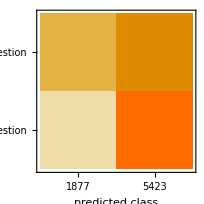

```mathematica
cm1["ConfusionMatrixPlot"]
```

```mathematica
classification2=Classify[<|"Not a question"->trainnonquestions,"Question"->trainquestions|>, ValidationSet-><|"Not a question"->validationnonq,"Question"->validationq|>,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cm2=ClassifierMeasurements[classification2,testset,"Accuracy"]
```

0.642329

#### Classify + Text Modifications

ToLowerCase

```mathematica
questionslist1= ToLowerCase[questionslist]
```

{she okay.,you know how sometimes you just become this persona.,and you don't know how to quit.,like my fear of wearing pastels.,what good stuff.,what crap.,19642,well what's the point of waiting.,it's sixth century b.c.  do you like the period.,dance.,okay.,what are you going to do.}
 |  |  |  |

```mathematica
normalLines1=ToLowerCase[normalLines]
```

{aaa!,aaaaaaaaaa!,aaagh!,aaahghhh!,aaaww shit!...,aah!,a b...,a b-24 liberator.,64118,zeke.,zerelda did.,zerelda it's no coincidence.,zero...,zero distortion sir.,zod.,zoe come say hello to your father..,zor-el but what can you a mere girl- superman will return it.}
 |  |  |  |

Random Sample

```mathematica
SeedRandom[1234];trainquestions1=RandomSample[questionslist1,13757]
```

{did ya get the license number.,you gonna pull.,we've known debbie what since the eighth grade.,joyce give the assistant chief inspector a drink would you.,13749,miss wollsten shares the room with you.,what do you want to know evan.,will these boards hold.,like my fear of wearing pastels.}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions1=RandomSample[normalLines1,13757]
```

{when he shot up that stranger instead.,it's about to be a broken face.,a cheap trick.,i fired her damn it!,13749,a compound organic-metallic alloy.,he saw you moving yours.,well lucy it's nice to see you're feeling better.,you.92d me amazed at how many of us there are out there.}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq1=RandomSample[Complement[questionslist1,trainquestions1],1000]
```

{how is gregor.,don't you think i know it.,miller no.,you get nothing hank okay.,how do you know how bad it was.,did i ever tell you i hate costume parties.,then i think maybe i'm just a victim of movies y'know.,i've had enough good news for today don't you open your messages.,what about that rock island bastard.,were you living with miguel alvarez in 1984 or 1985 when you had your anonymous sexual encounter in the porn theater.,bree what's actually happened.,and how do they explain your status to the client for chrissake.,what did you call me.,by examining the evidence from one case we might shed some small ray of light on the other.,did it.,how can he not have a heartbeat.,you're her boyfriend.,where is that.,putty.,why did he try to kill me.,like korben can i have 30 seconds of your time here.,well what have you got.,can i taste it.,what's funny.,but you didn't see it right.,do you believe that the world is coming to an end.,isn't it ridiculous.,are we here.,you're not allowed to speak remember.,who's next.,where's the name sheet.,no more questions.,where's the polk.,you and mel gordon.,nada huh.,who fuckin' shot me!.,what do we tell him about the guns and money.,are you doing some kind of science project.,you want my desk.,what shall we call him.,but it affects my ear i don't even know if i have tmj exactly but just very tight like - it's like a muscle spasm and it's just gets so clenched -- what's that stand for.,ten thousand.,i mean two guys doing the horizontal thing.,may i ask by whom.,what's it doing on a rifle range.,damn clarice how'd you make me.,the chink huh.,take him.,joanna what the hell is-- ted when we got married it was because i was twenty-seven years old and i thought i should get married and...when i had billy it was because i thought i should have a baby...and i guess all i did was mess up my life and your life and-- ted do you love him.,what they like then.,how could you have done that.,you're trembling.,have you got transport.,are you satisfied.,permanently disrupted.,what do you think was wrong.,why should he bother us.,where'd you learn to dance like that.,would you go up please.,what kind of school.,a job.,what was your father's name.,i mean is this really gonna have to one of those big brother -- little brother you broke my gi joe and i'm still pissed games.,what would your momma think.,do. jesus christ man.,lots of people worked for her she had the business from all these retail stores.,scared.,whose blood is that jay.,so he just said --  would you dance with me.,you did this -- overnight.,does the rule of english law no longer govern.,you got money.,is mom ever coming back.,why do you shamelessly waste my time like this.,you must have upset a few people boy . . . but that isn't really my concern is it.,is detective williams in.,where'd you get that stuff.,hey but did we get to you klute.,not everybody lies you know.,well what's the point of waiting.,you have bridge here saturday.,what have you two been doin' to make it look so nice.,oh he forced you huh.,what about in the mean time.,you didn't have a choice.,am i close.,a ride.,isn't that -- extreme.,are you looking for something in particular.,so your life's not over yet right.,shall we draw up the papers or is our handshake good enough.,did pavlov condition his dogs to lick his nuts.,there was nothing.,well sampson what is it.,you mean soap.,'cause you went out the back door and nailed her girlfriend.,what is it miss vivian.,-- we can talk -- yes -- all right -- can't we talk together reasonably just -- ordinarily.,was he ill was he sick.,and you wouldn't want to explode on the basis of false data would you.,do they pay you to screw that bear.,sometimes which.,you want this guy to come home fifty years old and he's still got that little pacific stereo badge on.,what are you thinkin'.,the hypothetical temperature characterized by the absence of heat and even the slightest amount of molecular activity.,i mean what are the three terrors of the fire swamp.,what crap.,she went to florida to retire like two years ago.,we're a medical firm aren't we.,aren't you gonna get undressed.,he used that.,do you remember a miss simms.,what's he got to do with your body.,i take the man out of argentina - and it was no picnic finding him y'know.,you mean that load of passengers.,for going to school.,could it be intelligent.,well what's the need anyway.,hawkins.,my man how you doing.,north.,you think i'd be working if i had money.,j what's going on out there.,who can play god.,and if you just happen to wash out i won't have to contend with you bitchin' to some hairy-chested female senator.,i just got out of bed and you're telling me you're giving me a goddamn speeding ticket.,what're you jaw-jackin' about.,mrs. kramer did you ever work in a job while you were married to your ex-husband.,a tooth.,who the hell is jimmy.,you have eastern european girl.,do you remember when we met at the bar. ...you were wearing a tuxedo.,this the guy.,maybe see where you grew up-- did you come here to tell me how to run my business.,should i be.,you worried she'll use me against you.,killaine's wise to what.,rose, rose, rose, you poor miserable little child, don't you know i love you.,it was just a matter of time till somebody fragged his ass and you know what.,did you tell joanna she should leave me.,did i request thee maker from my clay to mould me man. did i solicit thee from darkness to promote me.,fuck what the fuck is going on -- just safety your shit and get behind me okay.,so what are you gonna do.,but do you.!,is there anything we can do for you.,did you sleep well.,they hack into people's programs.,got yourself up.,what's in sandusky.,are the girls in bed.,andy do you know who reps kronos inc..,did you see what god just did to us.,where's clifford.,doesn't that make it our time.,no. 'didn't mention he was going to the justice department.,but what if that doesn't happen.,yeah who's this.,what is love.,ready uncle lex.,this is one of those interrogation tricks isn't it.,what's wrong kittle.,do you see me talkin'.,would you relax please.,what'd i say.,you think he's gonna be thinkin' about you.,who is on this committee.,and yet you chose to leave him.,guess who's here.,what do you expect.,and the golf shoes.,go over to her place and kick in the door.,you doin' any good.,isn't that true ilsa.,what the hell are you doing.!,how 'bout the sheriff.,how can they arrest future man.,were you adopted bob.,do you think if something happened it happened there.,which parts.,who's with me.,who's the other woman.,we don't wanna be alone forever do we.,are they lying.,better late than never right.,heehaw.,and an insurance pro.,but when you first came to casablanca i thought -- well what makes you think i haven't.,it's exactly... ...you wearing a watch father.,the sky.,how can this be.,sixpack.,what the fuck are you gonna do about it dickhead.,everybody savvy.,you love me.,you say asia can be found by sailing west.,why do you think they let us in on the deal.,what you got there - beers.,profit from major sales push -- minus .347.,what is the danger.,see-- this is what we do.,you've really got it all worked out haven't you.,first paycheck.,give a guy a break will you.,why can't he marry us on the train.,vhere....,how'd you get a tux at the last minute.,homer i'll see you tomorrow.,as an irredeemable criminal.,didn't you study six-dimensional geometry in school.,all in yellow.,like who, mr. chrislam.,you're having the best time of your life aren't you.,no no the grade...the grade that you're in.,so. not bored yet.,do they know yet.,don't you see a pattern here spuds makenzie.,wolfi who gave you this.,don't we.,can you assist.,you say to me boys.,what'd you say. ...screw you.,am i right leon.,remember that corpse washed up on huntington beach.,but you <u>were</u> having anonymous sex in porno theaters in 1984 and 1985.,what an important cause he's fighting for.,six people mutilated.,do i!.,what is money.,you mean you couldn't.,you don't want to say hi to your father.,mr. barton do you remember me.,i haven't by any chance grown on you have i.,you really want to make banal chit- chat like that now.,did you order our houses burned down.,any word back from the e.r.s.,you're not going to bust out baby oil and start rubbing me down or anything are you.,so tell me something where's the flaw in that.,looks like things worked out tonight huh.,haven't we honey.,must run in the family--you wouldn't be runnin' numbers out of this club now would you son.,how do i tell them that because of the unfreezing process i have no inner monologue.,you know that first day when i come and he said i looked graceful like a capital letter s and called me rosebud.,victor laszlo.,what does that tell you about the navy.,hey bad throat huh j-man.,what do you think i'm doing.,joey dorsey.,you mean that old woman i saw sittin' in the window wasn't norman bates' mother.,who were these people.,hello pinback are you there.,i mean bad.,don't you know any other adjectives.,you're saying one of those things lays all the eggs.,so i bring some cheese.,tomorrow is the day and mum seems to be the word and i can't have that now can i chris.,what is wrong with you. ...yah -- well at least y'know i got to perform.,me. am i.,'bout what.,taffey lewis.,which one pulled the trigger.,you come here.,know what i love about dynamite.,everything ok.,then it's war.,are you a fag.,see.  it's simple.,no calls.,tick- tock tick-tock how long till your witnesses fly the coop.,how'd you find me here.,listen you still want to go girl hunting tonight.,okay what happened right before he disappeared.,then you have some hot tea.,excuse me would you mind telling me what the hell i'm doing here.,trubshaw again.,can you forgive me for my wasted life.,done much shooting with that rifle yet.,what's the temperature now.,johnny.,sergeant.,for real.,i wanna see this...where is he do you know.,you don't see that.!,where do we start looking for this guy.,how are you dealing with it.,i made her feel guilty this morning --  brother what are you doing up.,did she tell you we had sex together.,whose dreams seem to be your dreams.,should call first you know.,i can't  clark already asked me.  didn't you.,so. joanie orozco's telling the whole school she's like desperately in love with santo guerra.,for when i travel.,hey no kidding.,good.,how can you not understand that.,is that an innuendo miss teschmacher.,do you remember the day i came to your monastery when i was a baby.,what if i told frank that you opened me.,what sort of questions.,so is buddy on your short list.,first thing i have to ask myself is is he playing for me or is he just plain playing me.,and how much is braces.,you're telling me it doesn't get to you.,are you sure it was that.,so could you walk on water.,did you see my father.,how much oh-two do we have.,how long was that.,you've got the files.,how was your day.,already escaped once from the max-slam facility on -- we just keep him locked up forever.,our little paradise -- just made for two.,all you gotta do is fix a few things for us  and we'll do the rest see.,can i go to jail for punching a guy who's been shot.,do you think you can dissect me with this blunt little tool.,so how'd you get caught.,you and verona.,if there was any other way -- that bad.,mueller was alone in the cabin.,should.,that phone message wasn't for me was it.,you mean <u>nothing</u> is worth fighting for.,why did they kill the guys in the other two booths.,and is it true miss moritz that you love victor frankenstein.,am i like such a fellow.,could you get me superman's autograph.,how camest thou hither tell me and wherefore.,why don't we walk to my dorm.,scott.,the police would know the difference wouldn't they.,it's a trip you know.,in over your head.,do you have any questions regarding the sequel of your life.,herr mozart what brings you here.,is he your husband.,he used to be a bloodhound but he's anemic -- what kind of a dog is he.,in a fire.,headquarters!.,how long i been out.,well i'm not smoking okay.,what's a buzzer.,i said did you really do this just today.,how about ann.,what is your will.,snappy name huh.,do we have enough time for a weld.,sure you wanna be havin' this conversation over the phone.,neuro charged assault model.,whatta you care.,what do you have in common.,the fuck you been doin' to me.,have you checked your platinum euridium energy shielding.,oh and could i get a quart of wild turkey two fifths of baccardi and a night's worth of ice delivered to my room please.,you gonna preach 'bout turnin' the other cheek.,evacuate manhattan.,is that your idea of a winner.,okay who.,that who.,what's he got.,me.  you're the one who tried to rip off this piece.,bunny you--uhm--you on that same medication.,justice.,what's the tv say.,have you seen a lot of movies here.,well he's the one shooting up all his guys right.,you going to have the time.,no what's wrong.,so it could have been neither of them.,do you understand what i just said.,decontamination -- .,could you not take some occasion without giving.,did you come here with wally--to *not* watch movies.,when is it finally going to come out that you were the one who killed him.,can those cops down there handle dr. lecter.,can you put men at all four.,why the two extra victims.,say who.,then why don't you take the job that louie netz offered you at boeing.,what's the running time.,about my blood work.,when did anyone on that paper give a damn about workers rights.,it is evil who stands here.,you married.,what was the warning of the thirteenth dalai lama.,cool.,why what is tybalt.,clean the slut up take her out huh.!,something bugging you.,quite sure you had no motive.,any sign of the goddess barrington.,you and your brother fighting fires together helluva image isn't it.,yes mum. and something to sharpen them with.,do me another favor. ...,others.,that your heart was broken.,made your million yet.,who are you please.,was it twelve o'clock.,you been with a girl ever.,why not against your religion.,then why weep for him.,you don't think....,so. what then.,how could you not *care* about the movie.,what did you say about a pet shop. ...what.,does he treat you fairly.,what's the matter baby.,we scared each other pretty good didn't we.,is her husband sick or something.,utah you copy bruddah.,that's so typical isn't it.,i hope.,it's not west is it.,i need your advice .97.97 something has happened .97.97 mr.  jacks .97.97 why don't you stay here tonight.,how much time have i got.,can i enter.,oh yes mr. klute -- won't you both join me.,just what would you like to know inspector.,are you there.,look if there was even one chance in a million it'd work wouldn't you want to try.,aren't you being just a little harsh mothershead.,resistance.,mademoiselle you are in rick's and rick is -- rick.,you don't swing.,frank gone.,that's what you need isn't it.,never been to maine before.,bonanza jellybean.,you two come together.,know any other languages.,of what sort.,me. bob.,so you don't believe his condition is the result of anything supernatural.,what are you doing herr director.,typhoon.,i'll think about it okay.,how else do you meet them.,you'd die for them.,and while they're burning up they're still goin' down on each other.,want a beer.,who did he go to meet.,i didn't kill him -- what happened to degrees.,another one.,you know how i spent last weekend.,how much will it be with my car....,bit of a pervert eh.,where's west's body.,are you mad.,have you done this sort of thing before.,blizzards in summer.,and you can see how you feel about me right.,would you like me to be there tomorrow.,and i don't want everyone thinking i've got tapeworms coming out of my ass or something okay.,how is your pretty wife.,what about jill.,you interested in a little work.,how's the new job.,translators.,why do you interfere with my little romances.,how could you be interested in that puny little girl.,and it's not real and you don't have to even like them -- you can even hate them it's all right it safe -- you know.,what and i care.,what if it's not bullshit.,isn't it due next week.,negotiation.,can i do something for you.,you're crawling around like a-- what are <u>you</u> doing.,they are.,if you don't want to be so appealing why did you touch the rose to your skin.,did you know that liz and i got into an argument the night she was killed.,where's my share.,dr. niko topopolosis.,when will you stop.,whatever's out there <u>did</u> flip over a canoe-- i beg your pardon.,strange voices rose.,you call the sheriff on that.,how about taking to uncle larry into the old firm.,when will strader return.,y'ever smoke any shit.,what makes you cry.,what the fuck are you.,we gonna crash.,it's not your given name right.,would you like one.,do you dream.,jesus christ jack don't you see that.,it's not too cold for you mr. penfield.,where the hell are you taking us anyway.,what are you reading.,if you knew it was impossible then why'd you waste my time.,whatta ya think that outfit cost.,could you have pulled that 210-pound man clear lieutenant.,and isn't there a movie in the works about you.,get what.,when will the stream be aweary of flowing under my eye.,do you really think i'm mad.,you ever think of getting a new car wade.,and do you amuse the guests.,do we know it's him using the beacon.,i haven't got the money so what are you gonna do about it.,what dead.,so mentally ill.,you miss it don't you jesse.,hear what.,what do you think it means.,why are you always leaving me harry.,no you're going to get kissed i know i'm going to get rapped in the mouth for saying this but so what.,you have a vacancy.,what is its antidote.,i mean do you want me to go.,does she have a lover.,what he said on the phone isn't important is it.,keep your chin up and your music down alright.,i am assuming you knew these two guys from before huh.,why didn't i just say something a year and a half ago.,moscow.,here wh-wh-what.,can't i just go with you guys.,what did you hear.,without her sensing anything.,what the hell's the matter with you jackson.,what the devil.,what's going on between you two.,elevated.,i have to go i don't have time and i have more drinking to do before i go march -- did you tell her.,does it float.,when will the wind be aweary of blowing over the sky.,am i going to england.,how're you gonna hide from a guy like that leave the planet.,you gonna make me finish that puzzle by myself or what.,he owned the colored roadhouse before big o-- bledso i told the story enough times--hell we were just in the car he was stewing about the fight with buddy while we drove over to roderick bledsoe's-- you don't remember anything else from that last night you saw him do you.,westley what about the r.o.u.s.'s.,or shall i come to you at evening mass.,you going rogue on me.,did you love your husband before you married.,and that's the job.,who wrote this!.,have you looked.,destroy your career over an issue of pride.,does it.,what's april 16th.,did you get it.  did you get his money dad.,don't you know this is exactly the kind of bullshit that makes people hate you guys.,whom have i been harboring in my house.,think a soul could get lost there.,how're you doing.,we drinkin' buddies now.,so how was the concert.,what was he after.,no of course not silly -- i mean felt like this about them.,what are you trying to do to me.,are you related.,what're we going to do.,will you give me a break.,do you understand the cards.,a soul's search: finding your true calling - are you reading this.,the deal.,should i get dressed up or -- .,so. i don't believe it.,what family.,why can't we pick up his signal.,disintegrated.,grounded for the rest of the year.,but what could i do.,and that's it.,danny it's really pains me to have to tell you this but do you remember domingo that wetback you helped us put away for trafficking a few months back.,la conner.,how 'bout a cut in your gut.,is she the kid you're gonna save from the burning building.,you like telephones.,do you wish him to be amongst us.,it's all over talk about what patrick.,i suppose you want me to fix that up for you too eh.,--<u>who</u> <u>is</u> <u>he</u>.,how much money can you lend me.,how could it not excellency.,he say anything about the summons i tried to give him.,what about luther.,anybody else have an idea.,filling in mother nature's blind spots ... .,supergirl.,the question's just been where to draw it bird flying south-you think he sees that line.,why's he called 'invisible'.,is that true or pretend.,jealous of what.,why didn't you mention it in your letters.,why waldman.,what's with the dip.,patty.,was she a great fat person.,but it wasn't all bad was it.,y'know what.,do you want to come to my apartment or not.,why can't you see my side.,why did you wait so long.,i mean i owe you one you know.,your birthday celebration your majesty.,turkish.,you think i got it.,why does that sound silly.,hey what do you think you're doing.,what goofy idea have you got now.,you're accusing mrs. peel of killing her own husband.,did he not already try to convince the king of portugal of his absurd notions.,why what do you mean dear.,i beg your pardon, epi-zoo-tics.,if you're up to it i've got us set up in a suite upstairs -- are we gonna tape some stuff now.,are you there hello.,we're supposed to be different right.,who's handling the scene here.,old howard winton's cub.,what do you know.,you mind punching a hole in the floor.,relaxed.,after that ass-whipping you gave me.,shall i be married then tomorrow morning.,valentin.,why do you do this to me.,should we scramble tachq for an intercept.,you still wake up sometimes don't you.,you guy's pretty good.,is that like us.,that's desertion right.,whose childhood friends were these.,how many could you handle.,how close did you get to that thing.,isn't that your jacket.,the navy.,yes mr. poe.,what is that thing.,wouldn't you rather know.,can you accept this mission and keep it private.,geoff.!,so tomorrow between 5 and 7 give yourself a hand that clear pal.,now where is that secret knot.,how much did you say it was tom.,explanation. ...,then who changed it.,what baby are you speaking about.,playing hooky again.,so me.,machine's in.,how did the rabbits kill him.,what is this herr chamberlain.,how you holding up wade.,oh what's that.,dorothy vallens.,what did i do last night alex.,i mean depends on -- would you have shot if it was a man.,well what was yours.,so what's your point.,toughened your nipples, didn't it....,who'd steal her body.,they killed some people didn't they.,you're a butcher.,get my crewies buried.,who do you see.,are you so hot.,i guess i was wrong -- phenomenal at taking bribes right.,m436  u6563 u6568 u6563 u6563 u6568 u6563 u6563 u6568 u6568  l377510 l377497 l377496 l377495 l377494 l377493    * sometimes you stop taking his calls so    u6563      * why not.,who *live* here in this cider house peaches.,whatcha doing in the underworld taylor.,that is simple isn't it.,find a lawyer.,y'see i didn't make her feel ok about that....i would say how many men you been with.,this look like a fucking post office to you.,a shower!.,so -- which dakota you from.,do you have a phone we might use.,who is he aramis.,should i give it more time.,lex am i gonna have to lock you in the trunk till we reach detroit.,your dad play.,but you hate joey he was like a total babe why.,that's pat verona.,why can't you give me your confidence.,and why do i think they're looking for you.,is he chasing us.,riddick please! riddick.,you got a problem with me.,do you remember the detonation time.,do you need a police escort starling.,and you are.,eve.!,truthfully.,what time did he say to be here.,buy you a drink.,honest.,what if i didn't miss.,will you hold still.,come on where's your pioneer spirit.,i mean what are you going to do about billy.,can you get this suitcase to her parents if you think it's appropriate.,i don't wanna sound paranoid or like a pig but what're the chances.,where's my wallet.,so what are these spanish guys like.,i don't get off and then -- eight o'clock.,think about what.,: what are you up to.,how long for.,you never heard of me did you.,so where do you go from here.,hey we can leave together can't we.,i'm a what.,tell me when we searched the place where were they.,did you say dude finlay.,who taught you be be a nurse.,can you think of a better reason.,while you were employed at wyant wheeler you did everything you could to make sure no one knew you were an active homosexual correct.,had goodness made me a good composer.,is that what makes it so delicious.,dunbar was running out the door.,but what reason could he have.,why don't you call the cops.,are you in trouble son.! ...and his church group have volunteered to help us bring the supplies down.,have you ever made love to a chigro.,claire.,you see the bullet.,what're your taking down.,what changed.,or this side.,with all this in mind mr. kross i can't logically make a formal bid on your company can i.,rehab.,which is it.,can i see him.,did andrew beckett say i might not be able to serve our clients to the <u>best of my ability</u>.,what about the money.,i mean no one's dealing with the homicide squad yet or anything right.,little guy's getting' hassled huh.,what does charlie mean.,before or after the explosion.,can someone call an ambulance.,elaine what's going on.,-- -- who.,are you yet breathing.,now can you help me find the complaint.,is she always like this.,you wanna be a big deal don't you.,did we tape the duke game.,what's the matter matt.,keep talking to that state trooper so he doesn't notice where i'm going okay.,why should she.,how big do the bears get.,you know each other.,know but.97 you.,we all set.,uh doc i was wondering if uh this evening i could come by.,you were smoking.,don't you have enough blood already.,you wanted to see me sir.,isn't mr. lowery back from lunch.,you looking for that place in the hall of fame.,can't you just force yourself awake.,such as....,i put like this techno beat on this japanese folk tune -- wanna hear it.,who is they.,how'd ya get him in here in the first place.,you do. ...no...no goddamn use.,staedert do you read me.,she figures they'll be so relieved i'm a man-- you met her family.,are these our two stars sitting here in front of my nose.,is that the manager.,have i ever told you about her.,are you sure this is a good idea.,you mean you haven't been able to get anyone at the base for ten days.,did you get a report from the m.e..,where'd you learn to do this.,convenient isn't it.,what is it they call you.,whatta you think.,is it like that with your counselor.,what'd you find kathy.,what's the problem officer.,numbers four and twelve directly into the nervous system.,make anyone cry today.,what's the matter with them.,where did you see her.,aren't you supposed to be buried in new york someplace.,reed what if we got these gifts for a reason.,have you ever been to bed with anyone else.,i've no choice but why risk yourself.,oh i suppose you is a doctor homer.,did you get fired again.,is he a fireman.,can you stay for a while.,raban did you say.,hey -- did these guys teach you to talk dirty.,does that check out down there.,state trooper.,you were able to arrange everything.,ya puttin' me on.,jack isn't that fred bliffert over there in the blue turtleneck.,yes . . . and is there something else you want to say.,which would mean lots of those parasites right.,you mean that you can't come here and i can't go there.,are you not feeling well.,now just relax okay.,guilty until proven innocent.,i'm of the opinion that these mutants will eventually kill each other off and then-- for how long.,you like me.,i've known him for years but he ripped us off -- and you know what that means, right.,do you want her to be unnatural.,them hands you got they know what they're doin'-- ain't that right.,me.,'bout not touching the switch.,does he wear pants this color.,next saturday.,just run now.,do you remember the last time you saw him.,it's sixth century b.c.  do you like the period.,is this your idea of humor my friend.,one: how did a celebrated life of the mind bring me  to this particular switching station.,what're you -- what.,we're going to give him the money back.,you wanna do what you do it's not a crime. ...you got my e-mail.,if i risk my neck for you will i get a chance to kill englishmen.,whatever made you want to do a tour down here.,you were holding it upside down weren't you.,how long have you been playing fraulein.,who had tank duty.,what flickering light.,i thought all our colonial scouts were in the militia.,go out the way you came in.,so what's the biggest.,who's frank.,-- ok.,-- the hotel -- how far.,i mean i mean i mean why did i fall <u>at all</u>.,don't this place look like home.,how do you feel jack.,she up for this.,which one is mantan again.,everybody go it.,it's friday do you have a date tonight.,how do you think she got the job in the first place.,baby crocs.,you've sacrificed.,what about your work.,you see a couple of minors come in.,and you're not.,did you notice the beaut that came in today.,what pate.,so...there's nothing you can tell me about paul owen.,good paulie.,ain't jemima on the pancake box.,but come on harry; what's the real reason.,you enjoy it.,does that help.,i'm not gonna let that bastard take my money double or nothing.,do i seem jumpy.,what are your plans.,why does she keep repeating the name.,why should it.,he was a year ahead of us.,or now.,provided that they can be assured of her ladyship's freewill.,is everything nice but not too nice.,syevodnya syevodnya.,any further thoughts on the subject.,did you hear about that prison riot last week.,the odessa dunk.,you mean in turkey.,right now.,what's that you got there, buddy.,fry.,take your ground grogan -- twelve paces i suppose.,i endured that as long as i could do you see.,more than three less than thirty- three--permanently.,then why doesn't he simply appoint me to the post.,you remember that.,may i talk to you.,how much did they cost.,braces.,does this have something to do with that man you saw.,can we just lie and talk huh.,how is it back there.,i'm just sixteen you know.,why do my joints still ache.,can you get him out of it eddie.,pick me up.,any questions.,well jesus that wasn't so bad was it.,then you knew of the inheritance.,... coming with me tomorrow.,do you think everyone that came back would be like gus.,brother and sister still.,you just drove by it. ...for three years.,to kill me.,what time did you make it for.,mrs. kramer do you love your child.,you want unpleasant.,real.,would it really put you out if they tossed that on the grill for a minute or two.,yes....,what should i know.,are you saying that someone is paying you to be our maid and doesn't want us to know who he is.,what's going on jim.,how's he doing it.,i should have called -- how are you.,you gonna steal my truck.,and who are you.,and who else but jellybean's wild cunts could possibly conceive of doing something so diabolical as to tamper with the last flock of some nearly extinct birds.,is this paper even good.,is miss dugan well.,who is to say our morals are better than hers.,i didn't bring any  -- your volcano chum.,you always been this selfish.,neptune.,so where is it.,is he handsome.,capillary dilation of the so-called blush response.,you believe him.,when's the next jumbo.,what do you mean me.,time to change numbers again.,big on the musical comedy huh.,why do you want to know.,what do you think of her honey.,ride a thresher.,so adam...where on earth are you from.,if you were the president wouldn't that put a little piss in your shoes.,where is vanessa by the way.,then why'd we tie him up.,the milkmaid's daughter.,the medicine.,i had to tell you right.,whatiya say we just enjoy the evening.,your doctor.,do you bite your thumb at us.,why should the truth upset you.,ah stephen that's what this is really about isn't it.,are there lots of uh rugs pieces of art stereo equipment uh furniture a lot of things bought with cash.,you mean a farm.,then what do you want.,are you sure. ...he's pregnant.,but -- doesn't god ordain both pope and king.,does it bother you to hear.,did you throw away those fries hamilton.,are you married.,are we safe.,what are you doin' buddy looking for a raise.,no they don't do they.,you know everything don't you.,mr. kent could i ask you something.,who knows more about maureen prescott than her own daughter.,don't remember what day that was do you.,you got her warmed.,what's happened.,why on earth do you say that.,know who i am jake.,is that woman a complete fruit-loop or is it just me.,you here again like an evil spirit to mar my happiness.,has the response picked up.,funny how things turn out isn't it.,where's the fuckin' beer.,oh well then i'm sure that's it he got killed by a dinosaur anything else.,do you have mrs. george for english.,oh excellency would you.,where's leeloo.,mmm. would you get me another half a-cup of coffee dear.,why didn't you warn them.,could we keep in touch.,what will i say when she comes to the door.,not much point to this is there.,you mean twombley.,what do i do if i'm not that.,of course i'm your attorney i'll give you all the time you need at my normal rates: $45 an hour -- but you'll be wanting a cushion so why don't you just lay one of those $100 bills down there beside the radio and fuck off.,has anyone offered you anything to eat.,who's ryan.,are these the answers.,how did you know -- .,do you understand that.,why are you bothering me about this.,television.,look ted i'm the oldest whore on the beat okay.,it's getting late isn't it.,what'd i tell you.,i was wondering how do you guys go to the bathroom in that thing.,who'd want to let in all kinds of riff-raff off the streets.,under <u>water</u>.,where's your manners.,what it's broken.,cynthia's not coming.,fired.,a tenant farm.,what's your bartlett's.,wasn't it keitel.,nobody did anything.,who do you know.,do you think i'm repulsively fat.,vould you be villing to take the siegfried oath.,to a 'formal picnic'....,nice to be married isn't it.,where'd you grow up.,what music.,have ya lost it woman.,why may one ask.,how much do you make now.,what's this roger.,how would you get him on land.,si--tengo escopeto--just a shotgun-- you carryin' a firearm son.}

```mathematica
SeedRandom[1234];validationnonq1=RandomSample[Complement[normalLines1,trainnonquestions1],1000]
```

{metallic taste to it human blood.,acting.,i'm sorry everyone but given this extraordinary turn of events i think it's prudent that we cut the evening short.,shut up sir.,so i can go ahead and be a historian without feeling like a poseur.i shall be fulfilling a citizen's duty.,but you can't tell where one country begins and another ends.,but  . . .,you won't dare to interfere with me here.,bass!,now get your tail out of here and go wash those dishes, and stop crying!,therefore i shall ignore you.,all the sharks have had laser beams attached to their heads.,good evening miss.,caught some son-of-a-bitch stealing my bike.,it didn't go anywhere.,clearly he was injured and bled.,let's get ya started.,he didn't either...at first.,i didn't know what to do.,you little pissant-- there's not a soul in this county isn't sick to death of your bullshit charley.,the opportunity was there.,we must have a blow-out.,when the nurse bent over him he did this to her...,i kind of fell in love with her last night.,i don't have a desk in my room and..,mom's going to hate it.,i want to let the gas run out.,so yeah i've got the sears catalog thing going -- and the tube sock gig  that's gonna be huge.,with all she was doin'.,in a minute.,he mentioned a name at the very end.,i'm not screwing around.,old ties are hard to cut.,i suppose she addressed them to me in my real name by which i never thought to ask for them at the post office.,no you get out of here.,he'd be all right.,haircut.,bored.,babes.,oh naw.,oh there might be something stashed away for emergencies.,and i think you should talk to him.,if they could get her to give back the money..,in that case we'll need to make it a school-wide blow out.,but ah... ... after his wife left him and he was taking care of the kid on his own things started to change.,i'm not callin you big black africa.,and there may be a way.,it's a traffic thing.,the nuns got off easy.,you're right about that guy chief.,yeah i heard that.,many worthy of attention; but valuing is something more.,that's none of your bussiness. i have been a good worker a good and loyal worker for you you fucking asshole.,oh but if jan should find out!,c'mon, frank.,yes i am.,charley was one of your old-fashioned bribe-or-bullets kind of sheriffs he took a healthy bite out of whatever moved through this county.,you down with delacroix.,we recover the money in cash and let the insurance cover the corporate fraud.,sonofabitch wouldn't accept it.,if a thing's worth doing, it's worth doing right.,cold.,and this is china.,if you hadn't found it it would still be lost.,looks don't concern me maestro.,you barely know them.,and he has a really hot ass with hardly any hair on it.,logan cale.,awww-rr, buddy, come on, you know me!,i saw your car.,who cares if you're never known as the first girl in the nba.,well majesty it is only a comedy.,okay let's get down to it.,they found the drop car up on mulholland.,i hope ya trounced her a good one!,now's the hardest part, starling.,you understand that! ...,mommy and daddy named you julius.,gosh!,management were pin heads.,kramer i'm sorry.,oh all right.,i tried the hotel.,i don't scare that easily.,this is a six-shooter.,that's always a good sign.,right here baby.,pipe lines stop pipin' oil.,but that's your problem.,magicians do it for real.,stay right.,i've been better..,i'm *not* a doctor!,and in studying you must have learned that man is mortal so you would have put the poison as far from yourself as possible so i can clearly not choose the wine in front of me.,i'm having one.,louella parsons is here.,hope you're carrying some protection.,you know the guy who did the weismuller through the window -- home.,least of all me.,well he sure as fuck knew you!,steve said you were thinking of leaving.,we almost had an accident today.,god how..,i could value only someone whom i loved.,it's like i could spend my whole life thinking about it...,maureen tries her best to detach herself from the movie.,i'll use the chair here.,it's gone.,this has been one very fucked up job sam and i'm not taking any more chances on anybody..,got a cot in the back- people get afraid to go home they can spend the night.,i can't afford to make exceptions.,goddamnit joanna.,i already got that department taken care of...,i know i'm not exactly a girl scout but . . . maybe if i show him i'm trying . . . he'll like me.,it's a perfectly good car.,meaning viznick's a man who answers to no one.,but i want the fairy tale.,me and my bunch hit a dealer in the middle of a sale.,come on you're prettier than that.,no movie.,from basketball.,this is the mother of my child-- i thought you were married!,you'd better sit here and keep warm while i go for help.,l627561 l627554 l627553 l627552 l627551 l627550 l627549 l627547 l627546 l627545 l627537 l627536 l627535 l627534 l627533 l627532 l627531 l627530 l627529 l627525   l627524 l627523 l627522 l627521 l627520 l627519 l627518 l627482 l627481 l627461 l627460 l627459 l627447 l627446 l627442 l627441 l627440 l627431 l627430 l627415 l627414 l627406 l627405 l627365 l627364 l627363 l627362 l627361 l627360 l627359 l627358 l627357 l627356 l627355 l627354 l627349 l627348 l627347 l627346 l627345 l627340 l627339 l627334 l627333 l627331 l627330 l627329 l627328 l627327 l627326 l627325 l627324 l627321 l627320 l627318 l627317 l627316 l627315 l627310 l627309 l627308 l627307 l627306 l627305 l627299 l627298 l627290 l627289 l627141 l627140 l627132 l627131 l627130 l627129 l627128 l627127 l627061 l627060 l627059 l627058 l627057 l627056 l627055 l627054 l627053 l627052 l627049 l627048 l627047 l627046 l626982 l626981   m585  m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585  harry simon harry simon harry simon harry simon harry simon harry simon harry simon harry simon helen voice helen voice helen helen voice helen voice helen juno juno helen juno juno helen helen juno helen juno helen juno helen simon helen simon simon helen simon simon helen simon helen simon helen simon helen simon simon * say.,it's shit.,if you're good enough to get in here and handle the gear you're good enough to know you don't need this.,in there sir.,give me another.,that's the one i'd've picked for you myself!,ask them what the candles are for.,right..,why that's the speech that lincoln made at gettysburg..,that's all she fuckin' wrote!,oh i fell on my keys.,we cannot.,like it or not this is the only oxygen for three billion kilometers.,second rank!,these observers were doing something.,hence the radiation.,goodnight little house.,i guy i know used to use it for his bigger deals.,blank faces here o'neil.,we advise identification possible.,she's in california.,you're my handsome man.,so he decided that one be put away as if he never existed.,you've had it.,but then i lost her.,i don't need this to hit the press.,yeah i know you have to work the whole time i'll probably have more fun here.,i think you've got termites in the house.,would you stop with that..,not as the baby they took away but as a man.,we've been trading off nursing you in shifts.,alright alright cut it coolio.,these aren't just..,you've had plenty of time to fix him up and he's leaving with me now.,just the facts general.,he could read people so chance had nothing to do with it.,uh...apone i want you to lay down a suppressing fire with the incinerators and fall back by squads to the apc over.,but you should check your backpack 'cause those guys like to steal shit.,aramis..,let's drop back an' boot up.,thank you royce.,we'll never finish the other three.,for whatever reasons i thought you might be more receptive.,i'm still editor of this sheet.,uncle this is that villain romeo a montague our foe.,i found one of your letters..,let go of me!,i've always hated you for that.,friends don't help other friends cheat.,i learned it from my guru the late guru shastri a chaste man who mysteriously died of a disease that had all the hallmarks of syphilis.,mr. balboa -- ...thanks.,she's afraid of the hospital.,i'm fine!,he just fell asleep.,and picture the birds doing their sex dance on tv.,she lives on the seventh floor.,and it just sends you someplace.,get to that chopper and hold it for us.,but i got a client lookin' to score some fire power.,somebody's in a vengeful smiting mood today.,it's our only chance.,he was losing weight.,just give it a try.,i just need to lay down.,conglomerates're lined up to finance the launch of the remaining satellites.,let me guess you're a...,i'm a girl who's in a jam and it's your job to keep me there.,i fear not mrs. kendal.,she's a good lady.,that was in style a couple years back man.,he's not gonna be happy.,oh those.,but there is worse.,how she treated you.,it seems right to us.,and you're a terrific chess player mr. danvers.,someone's trying to get out.,then the whack club i'm on loses three games in a row and i get blamed.,well i'm just an old dame without much time left so you'll pardon me if i jump right in here before they discontinue my blood-type.,claire used to tell me i loved the event horizon more than i loved her.,havanas.,maybe we'll come by tomorrow help you clear up or something.,i want to examine the crew.,but doctor that's an active case i'm not involved.,one cervical stabilizer two sets of dilators--douglas points.,for all they know..,anyway he was at her apartment a few hours before she was found dead.,somebody must have seen it.,they certainly take their lives in their hands.,it looks like we're following him.,we've got to get ready before he gets here.,buddy was more a part of the big picture--county political machine chamber of commerce zoning board if i kept those people happy he was pretty much on my side.,yeah i guess i'm still a little mad.,wallace has sacked york!,c'mon jimmy snap up snap up -- and the book says: we may by through with the past but the past ain't through with us.,general jim beam then.,help me.,that doesn't make any difference.,and i moved in with lydia...,no but i passed by it a couple of times.,what you saw tonight, we're not talking about a video some dentist takes home over the weekend.,but would you stake your life that's the question...,we do it the hard way.,i even had to pawn my diamond ring then.,tell them i've got my own reasons to be very interested in whomever did the job on the nuns.,i say we take off and nuke the entire site from orbit.,magua's way will bring only sadness and shame.,you're about to become the anti-christ who is born unholy and becomes the door to eternal suffering in this world.,remember a jedi's strength flows from the force.,there's food in the fridge.,i know the law.,i saw nothing.,i'm sure i must have been a great disappointment to her.,what it means in england -- and in scotland too -- is that rebels have forfeited their lands.,well i gave 'em a taste of american lead ... and i don't see 'em coming back for seconds!,i'll call my study partner.,ay me!,they couldn't go doing everything at once.,we didn't hurt him...,now look darlin' this is no time to go off into the fourth dimension.,and i suppose dr. murnau didn't die in a cave-in.,stuff like chat.,too good.,or sometimes not at all.,you won't believe it...,binoculars.,i'm stopping it - slowly.,almost through.,well don't give up now slick.,we'll just sell another baseball card.,you and your real estate.,homicide miss hearn.,it doesn't ring a bell.,i came on my own.,i happen to know that he gets ten percent.,no we got pressure from california state.,i've got a kid.,the king has mountains of gold!,fedorchuk couldn't find his ass with his hands in his back pockets.,similar but not the same.,all that you gotta be vicious stuff you filled her head with.,hardly two stories in the whole place.,don't even try to play it like you ain't a part of all this.,cici.,we got us a tent forty-two feet across eighteen feet at center hundred-and-ten foldin' chairs.,and you don't even do your own product!,but no one heard so i just stopped shouting.,wait...don't leave me in here..,i'm a little scared of storms.,john will be very excited.,a joker to the end.,the place produces nothing.,then swede and i split with the package and meet you back at the rendezvous.,yes so what.,you don't need to screw around anymore.,i used to play ball.,now - let's talk this thing over.,she uh...,like i said i was freaking out.,when i ignore you that's when you worry.,our kh-ll's took this one at 0100 hours.,i only hoped that your knowledge - oh officer starling...,don't you even think about it.,thank you!,but keitel if erik ever finds the horn resounding..,there are a lot of command ships.,taken together that's gospel.,drink heavily your feet will know what to do.,met her on the train.,aw shucks ma'am...,'my wife returns from europe tomorrow.,you'll know what to do.,bubba.,we all came from africa supposedly.,his name's jones.,i love the way you've arranged your pictures on the mantlepiece.,they're going nuts for these guys.,a good shower that's the ticket.,you send me a scrap of paper -- and we have a scrap.,i said...,good idea!,when i took off lady cosgrove there was no man of my years who looked so young as myself.,you're my conscience.,conklin had these guys wound so tight they were bound to snap.,i out that gun in my bag deliberately.,you know how like they say you save someone's life you responsible for them.,it's not enough that i succeed.,i'm not ready to grow old laz.,she was there...,you didn't listen to people.,trust your own judgment.,like i said-- this isn't my regular line of work so i'm making it up as i go.,you killed him.,you're dead you're fucking dead elias!,i've got cobbie downstairs watching the door.,you go full auto on a guy from close range you're gonna be swimming in blood.,they got all kinds of high-tech shit nowadays.,just doesn't make sense.,in case of emergency!,a walking penis capable of intelligent speech.,thanks for your help.,this used to be the main highway.,get away from me!,satan is not what you think he is.,they don't hold him for more than a day or two.,slamlight's so dim that you go and get your eyeballs taken out and shined up -- then you wind up here.,no you don't know what it is.,now here's what's goin' down.,now for the fire.,oh ... that.,yeah right!,just don't tell anyone i have a soft side.,she's perfect perfect.,prisoner discharged whereabouts now unknown.,bill -- bill -- bill is out there..,those which stir the imagination as well as the intellect.,but i'm the one in charge of her sorry ass.,give men that.,jennifer doesn't know.,i thought i should bring it to you.,back when buddy had it-- hell i'm just a jailer.,that's a disgrace the guy pulls a gun on a cop and he's out in 24 hours.,and i was wondering...if...if i could have a...,a hundred rubles st. petersburg hits 95 percent in a month.,i'm an orderly not a bleeding psychiatrist!,anything.,guard the shoreline.,they were quite insistent on this point and said they must have absolute assurance of her ladyship's perfect freewill in the transaction before they would advance a shilling of their capital.,that's very tempting but it's impossible i'm afraid.,you don't seem excited my little muffin.,get that doctor.,you know i respect that you have such faith james.,she's amazing.,sorry occupational humor.,well i was going to wait until after the inquest...,to perpetuate such creatures is to celebrate their crimes.,you know there's like this rule.,i want you to just keep that in your head.,this isn't gonna be easy.,she was a real asset.,if we act too anxious, he'll make us wait.,but maybe you better let me take over.,i figure.,the fit isn't right.,i - i really cannot do that your excellency.,then i wasn't beautiful.,that's how come i told you about it.,mr. bialystock.,if you just radio base and let them know they'll fix on that.,in twenty hours we run out of air.,i knew you were crazy.,let's have a toast.,it takes a while to figure it out.,you've got to show her respect you've got to show her that you're not like joe..,maybe she's not over it either.,we are fucking dead.,i wanted you to have it for your trip.,lord forgive me..,between the girls.,ah well i think i've found the malfunction sir.,she has other things to do, dave.,he doesn't belong on this mission.,he knew he was gonna get caught!,then he said that the world was coming to an end.,girls decide how far to let you go in the first five minutes.,mr. gorman just answer me one question..,he was pretty much dead.,i'm not good at being alone.,usual bullshit.,i can't get it until monday.,he can't handle the medicine.,well destructacon 5000 you have quite a head on your shoulders i dare to coin.,we don't know mary.,i can even stitch in a pinch wouldn't be a bad idea here.,you have to be good to do that and if you look out of a front window of the empress hotel in victoria in a few hours you can look right down on mr. brandon's boat the valkyrie.,my goodness.,but i do not see men on the end of nooses.,which reminds me i need some new kicks.,benoit a landlord...,this is no dream.,you have enough problems of your own.,it's seven o'clock and time for the news.,evidence.,it's 'till death do us part.,i think about that.,i knew her.,his parents are both at work.,you shut up.,supreme court.,i was misinformed.,i'm sure it doesn't bother you at all that it sounds like ss'ai k'ss two words in my language which mean excrement and cranium.,well i should probably get going.,god would never allow anything like that to happen.,he's trying to jog your memory.,here's some money.,i don't know newt.,you wanna have your way you take it.,you gotta make him do the start-up with teddy and me.,one country did sponsor the resolution.,you got three minutes.,he must have been a very powerful man.,this was mrs. lippman's house.,check the eyes ben.,and a model.,a few things came up.,i'm a traditional guy..,no nothing.,twelve hours!,you seek facts when it would be better to seek truth.,no don't talk like that son.,now i'm telling you again, get off my lap.,it blew up.,twenty bucks.,ok.,she isn't anybody's friend and i don't like you living with her.,gov want to leave me that one.,this has nothing to do with you.,you'll have to get right on it andy we're up against the statute of limitations.,i did...,they are under your protection.,that was before twombley was shot.,i've never worn the same pair of socks twice.,everyone's saying he's . . . dead.,deny thy father and refuse thy name; or if thou wilt not be but sworn my love and i'll no longer be a capulet.,i start fires when i'm angry.,i'm sick of working for that dickhead.,jesus mercy that's charlie higgins dave laller ...,he has educated feet.,then we shall state another time and another place.,don't fuck with me man or i'll blow you into tomorrow!,the first to touch it will be the winner.,tooling along the main drag on a saturday night in vegas, two good old boys in a fire apple red convertible...,and my does he hate us!,to tie it all in to gary.,the pitiful son of a bitch said rose was a nymphomaniac.,i think you were wearing that black dress y'know with the buttons.,please sit.,maybe they never got here.,oh christ!,christ it's oil of tansy!,jake you play the heavy rackets like that..,i'm not anxious to find out either.,the bastard deserves to die.,he could actually do musical harm to the princess!,goodnight monsieur rick.,whew!,this is adam.,i'm a ballplayer okay.,replace the king.,come on with the rest of it.,i can hit those boys from here.,i like 'em.,by the hour of nine.,we're even.,what i will do is keep names out of it till we got some answers or hit a dead end.,it means nothing.,it's their presidential suite.,i don't care if my clothes are taken seriously.,see you tomorrow night.,and he took his money with him.,here. 23rd street subway station.,listen it's not erasing.,it's isolated.,i can help with the eastern european angle.,the kind you tear up and get rid of.,i no gotta new-rosis.,all the blood money you had to move around to make this deal you got to know something.,which leads us to..,tell him if he would that would help me finish it.,they really applauded you today honey.,get me a couple juicy pictures.,i was wrong!,i haven't seen anything like this since the lina wertmuller film festival.,i don't know how to walk in heels.,it's hard to l-a-u-g-h when your father's dying.,perhaps we ought to stop now.,not every man really lives.,obviously so.,it'll be okay baby i'll hold your hand.,knows it's fatal.,but johnny...,all the pumps!,well my friend and partner was shot last night and i'm after the shitbag that did it.,god doesn't...,i left them here.,no mrs. lowood she doesn't write often.,and you want to tell me you saw norman bates' mother.,which involves you.,calvin i wish you would have at least let me do the dishes.,we must have faith.,rick i really think i'm in love.,you'll never get over it.,i just hope she isn't too much for him.,we need you to prepare a detailed briefing on the ship's systems for the salvage crew..,oh but i just told you.,in other words the whole goddamn world knows you're here!,myra.,nix has got to have a weak spot.,i hate her guts the bitch.,like you said mr. deckard a machine can be a hazard.,go high in the ceiling.,smells things that ain't there.,don't blow your nose!,just squeeze.,we'll find out when it goes bad.,nobody gets invited to clark brandon's parties.,i was a sorority slut.,my secret lover.,you have no idea how awful it is to be mean all the time.,i don't know...unsure.,there is a price to all this required both by longshanks and our nobles.,it's a joke.,he hasn't used any of them.,bunch of goddamn adrenaline junkies.,i won't have him back.,here follow me.,you people knew this ship wasn't ready to fly.,yes, now i'm remembering very clearly because i'm picturing.,killaine's wise.,let's...,i was recommended.,that arm you got'll get'chu on a box of cereal...,i wanted to come here.,listen the last time i admitted to a woman i loved her ...,i was sure you'd  l377601 l377600 l377599 l377598 l377597 l377596  u6563  u6568   m436  m436 l377590    teddy leonard teddy leonard teddy leonard teddy leonard     * like you've told yourself.,it's a real good chocolate cake.,i'll make a deal with you!,we've made some amazing strides in digital convergence.,well there it is.,thought i'd kill two birds with one stone.,but that's cheating!,i thought that earlier in the diner.,joel come here.,all right thanks to her and thanks to this case of epizootics you are getting another chance.,being his son all you had to do was breathe to graduate here.,let her know.,i was exhausted and could search no longer.,richard dear i'll go with you any place.,i don't think i'll be having sex ever again.,anatomy.,for most girls seeing the bolshoi ballet would be the experience of a lifetime.,true story.,how many times....it's ok...just say...,if the company felt that you or your crew were in any danger we would authorize an immediate emergency pickup.,look ma no wires.,they also found my two beam scale in the garage.,'start-up not 50 miles from here.,the night we had together..,i took one lamb.,i can zap a thousand chernobyls into the air.,you and i both know sometimes, not often, but sometimes there's real reasons why a kid'll run.,don't talk to me about elaine.,i mean if anything happened to me he'd be okay with you.,mio caro adone.,tom the fatter you get the sadder you get.,they put butter on everything.,i chant.,our paths through life must be righteous.,i am one lucky guy.,oh and make sure they send a helo with a winch -- door's blocked by a reef.,and i don't want you here.,and what you're into i'm into.,no but he heard firing just east less that a kilometer.,last time they won dr. j. was a nurse.,yeah you had a piece of pussy on a plate in front of you you'd probably kill it.,maybe we should call the coast guard.,i don't know nothing about it.,there's two cops outside that want to ask you about this -- i'm a little busy right now -- investigator...,you are home.,-- you should meet my father.,two in the back of the head.,it's only a physical problem.,let's go!,i wish you wouldn't pick on rose and tease her like that.,when i was sittin' behind a desk in washington it made sense somehow.,she sings little peasant songs quite nicely -- a completely untrained voice of course.,call me tomorrow.,skull was intact no soft tissue left--not much to go on.,i daydream.,the book again.,please don't jump on me.,we're just walking ghosts to her.,all this traffic new buildings prosperity..,and a lot curious.,oh your excellency i don't know what to say.,it's only majestic from here.,gee.,inside there's a silvery ring..,and i understand why you might want to think he could.,you never gave up.,my spouse's brother is one.,when i used to have nightmares.,that's not a spear.,i don't understand it.,what're you implying.,right in front of us.,this is not good place to stop.,doesn't want to mention her name.,she was seen leaving town in her car.,it's gonna be gone soon.,but when he tries to rescue a woman he's gone soft.,you don't work for interpol sam.,it's a rob roy.,if you know a way out of this place and you're holding out -- easy.,he has managed to alienate practically the whole of vienna.,coppery.,that's fucked it.,you look frightened.,i have hurt your feelings.,what happened today's just the beginning.,oh i do...,thought you might be interested.,well you don't have to be so dramatic about it.,i noticed your hair.,semen.,i'm plagued with my share of difficulties just at the moment.,help jamey look.,practice is only on mondays and wednesdays so...,start over with a clean slate.,other than that ask what you wish.,dave schapiro is no horse doctor and rose has been a good wife to him for a long time.,angelo we gotta talk.,just get in yours!,that's the old rick!,hammond.,i think she was crying..,now she can return the compliment.,we don't get the power back our air's gonna go bad.,poor man.,papa's right - i should put a padlock on my mouth.,yoda i must know.,the date's not set yet.,i didn't recognize you.,let's waste him.,honey this is my son delmore.,don't worry she'll tell the face to beat it.,and make the huron great.,but you can't forgive for liz.  no one can.,but no, you can't be sure about a thing like that.,the car seat that's one thing.,i'm not going anywhere.,and i didn't like that man.,i've slept enough.,opening pod bay doors.,gonna suffer you like jesus say to the faithless and the perverse generation.,okay i guess.,your husband on the other hand...,so have you.,i'm just procrastinating.,it's how i make money.,father's looking for you.,and i'm not young anymore.,back!,he got what he deserved.,well of course she feeds me.,they got it shoved in their back door.,that's what *i'd* come here for.,i want a guy like you for real.,three four.,i don't think it's gonna matter.,you'll probably squeak by.,get up!,firemen don't carry guns.,i was a hostess at this club your daddy was performing and i had never laughed so hard in my life.,no it's different honey.,alma i think there's some dirty business going on in this town.,i know he's at work tonight.,within a minute harry lost his temper and reached for the nearest thing at hand which happened to be a fifteen-inch black rubber cock.,yeah but come on...,it's got him.,uh . . . no man.,i dreampt my lady came and found me dead and breathed such life with kisses in my lips that i revived and was an emperor.,you caught me playing hooky-- i always wondered what you mayors do when you're not cutting ribbons.,so alive and spontaneous and passionate and sensitive.,i see it before me.,doing great mom don't worry about me.,it watches you.,i'm fuckin' done.,that's some good shit.,i've never heard..,but <u>i'm</u> the messenger.,if we could just talk about boys everything would be so much easier.,there's nothing to think about!,mr. penfield.,i had nothing to do with that i tell you!,max!  and you can call me leo.,here they are.,i'm waiting for your mother.,i wonder..,that bastard.,dark valdez.,ted all i wanted to know was where-- i came home tonight.,i've seen them grow up in the community.,and that royal cousin hanged a hundred scots even women and children from the city walls.,curiosity killed the cat.,we could move on.,we'll never survive.,i want to die...,do we talk about this..,why don't you get undressed.,you don't know him.,till i found out i was wrong.,you can suck a fuck.,vacation.,if he does it's his own fault!,he was talking to me and leon about marriage.,mark it mark it!,i said goodbye to you.,-- so there were two of these explosive charges placed on the power lines.,take her.,no that's fine.,atta-go.,if you're going to be indiscreet i wish you'd be a little more discreet about it.,'cause we got more important things to do like finding out who did it.,there's some vodka in the freezer.,you'd be surprised what horrors a man is capable of.,not that interesting.,gots no intention of ending up broke.,your plane's at nine a.m.  be on it.,i asked you to keep your trap shut!,they're dead now.,plus to minus.,i'm terribly sorry.,i never thought it would end.,perhaps an arrangement can be reached.,sir we really need this job.,therapy session is over.,i scoured the city for it.,it's too erratic.,from now on no more pizza!,my wife needs space i don't know my kids ' birthdays.,time i've got plenty of.,i'm just a bit of a wreck.,you know, every pageant is special, but this one is extra-special to me.,i guess i always will be.,so you're not too different from him or the chap on the roof or tommy-baby -- mm. ezra i'm lots better than you're used to.,you look thin by the way i've mentally undressed you i can see your ribcage.,forty-two-hundred i figure.,it's soo good to see you.,cornelius..,we'll meet at debbie's tonight.,i've been looking for that thing!,you'll make it outta here.,this is hardly a time for levity.,fires the eighty-eight.,oh comme si comme ca you know...,all these years i've known you you could never wait for anything.,i just thought she might not wanna meet her maker lookin' like a cheap whore.,if you see someone who's gambled here even if it's just casually on the street you must ignore him.,i have work to do.,please don't tell mom and dad..,dr. neilsen.,you think you accomplished something...,he is the courageous captain of compliments.,to me it shows part of our history in this country a time when we were considered inferior sub-human.,you john-wilkes-booth-ed him.,thanks guys.,i want to be called fran.,go anywhere do anything.,and live with me in a storeroom behind a hardware store in fairvale.,stationary with bates' motel printed on it in case you want to make your friends back home envious...,i was just showing homer the orchards...,up to now, you've always been associated with musicals, and...,but my fears were to prove groundless for on that very night patient nature would claim her account.,i know you're probably at toby's but i'm in bed reading.,don't tell me you've changed your mind.,thinking that.,he's after your money.,let him get some sleep.,you follow directions well.,we need your expertise.,we need all the help we can get.,it's delicious i think.,not enough for you to hear what i'm sayin' you gotta understand.,but i have a couple questions that i wanna ask....,it was igor at the waxworks.,money is no object.,ugh!,i'm not really.,i hate you!,ask not for whom the telephone rings ...,i never told anyone until now.,that's...,well you lost me with the last couple of cocktail words spoken m'boy but i believe it's that sort of love.,all she wrote.,you are . . . nothing.,and..,now let's get those knees up!,and the second was from my lawyer telling me he was leaving too..,standing ovation.,foredecks.,this guy is very sharp.,no - i've got a sweet-payin' job that i'm about to lose.,i been with him all day and he loves me, i know he does, he loves me and he's going to marry met be's practi'cly ast me already!,children children!,no but i have the feeling i'm about to find out.,he's just a guy who's got a nose for this shit.,at least call!,understand the carving and you will understand the people!,it's not who i am.,not to my knowledge.,you don't choose your dreams.,kitchen. . .,i'm designated driver.,great story.,just ring linen service and ask for alice.,heading three-three-four..,i was up all night cramming for this physics test and i was putting this little baby together.,besides -- when you let the enemy think he's orchestrating the battle you're in a position of power.,but rimgale's probably going to come around to arson.,you owe me an explanation.,i can offer you god's forgiveness.,he'll double what i pay you.,now i'm free of it and i'm gonna stay that way.,until ma has you home so she can fuss over you herself she's gonna make me miserable.,you're very valuable.,they won't understand you anyway.,the decision is final.,and when you said to look for signs of aggression...,and you didn't say anything.,i'm leaving casablanca on tonight's plane the last plane.,that's easy for you to say bianca.,watch that one he's an ex-spook for sure maybe stasi maybe kgb.,these are stock certificates that we bought in your name.,anger fear aggression.,hi helen.,kept calling it murder when i did it.,you were gonna get a degree maybe somethin' in business or agriculture and you were gonna make somethin' of yourself.,i feel like such an idiot.,i think jeff bridges is getting tired.,here pick these up!,people callin' all the time.,if that's not an insult i don't know what is.,not hard to find you...just follow the chaos..,god saw to it to put you in my path.,especially for..,this fellow lives like a hermit..,no it's him!,because he knows what i know -- that american families are not prepared to put their daughters in harm's way.,i'm going back to new york in--  shit!,noooo!,it was the please that caught my memory.,welcome ten thousand times.,my leisure serves me pensive daughter now.,i can't read.,you got a deal.,snap out of it bomb.,only the heads.,problem my ass!,i'm with the l.a.p.d.,vader will destroy her.,you let him get away!,i think wally will be fine mrs. worthington--he seems indestructible to me.,he's too busy rushing off to philadelphia to make stuffy old speeches at stuffy old bankers' meetings.,he's climbing the rope.,we got a kid at tailback from down your way--outta el indio-- he never asked her.,then we will both be free.,find out who a.d. is.,but if it wasn't for dignan i probably would of died.,'night marie.,i'm different.,this night you shall behold him at our feast; read o'er the volume of young paris' face and find delight writ there with beauty's pen; this precious book of love this unbound lover to beautify him only lacks a cover:,i could tell you were sad.,yeah brothers are lined up at my locker.,it's the model you've been saving up for.,right here.,wrong answer -- dunbar's telling the truth.,more light and light more dark and dark our woes.,never saw him was your basic hit and run.,want to fry the whole goddamn world.,you cannot escape your destiny.,about a foot away.,the plans for use of the maze were not disclosed to me.,numbness.,frank ligourin.,you could still help me do that.,wouldn't dream of it sir.,please don't.,see what you don't know is you're already in the last two minutes of your life.,preferred being the geek to having to explain.,i'm a law suit.,he ruined it!,hurry the fuck up!,oh god i -- forgive me...,uh...uh..,and his 'egghead' son!,i know you're as unhappy as i am about debbie's marriage to rick.,that doesn't mean a damn thing.,you just walked through the door.,i don't know that i ever even had it to begin with.,no i mean ours motherfucker!,i like your hat.,we believe that when they die he takes their money.,that's all i wanted.,we showed our ass in texas.,oh god you don't know what you're asking.,appipulai leeloo minai..,about yourself- ah i see..,oh save it.,it's about these toys.,hey i got it!,family wants to forgive her...,follow orders.,you've got to do something special.,well ask her!,just be sure you spell my name right.,he's a fucking psycho.,we're losing pressure at 280 liters a second and our oxygen tanks are cracked.,he's out of town.,you'll tell them a simple story.,see ya around.,i couldn't do anything...always scared y'know...,i object to a cut-rate one.,so i say mush on!,it's a contract violation!,i've discovered something interesting charles.,all right enough!,picked over, ten months ago.,and if you're cute and horny..,i'm looking for -- seven years work by the finest engraver.,so did dan.,if i found jimmy hoffa on national tv, i'd still have to retire in two years.,you don't like it quit.,fuck man!,you're pretty much all healed up.,he thinks that i am a gentleman and that you are a lady!,and lo' and behold as the husband of a person's grandmother is his grandfather i mantan became my own grandfather.,i'm going to get even with you you dirty stiff!,guess i'm on a roll.,and then he spoke of a girl of surpassing beauty and faithfulness.,i'm the guy in your bed the last three months.,i think he has his own plan uncle lex.,put your hand down.,legs butt and hair.,jesse james never yelled at folk..,big o's is the only place in the county that our african american soldiers are uhm--that they feel comfortable in.,i don't know who i.97.,they could try to tranq him on land.,i'm gonna go get the money.,roll the hose.,we're here to stay.,paul wasn't into that.,half mile up, there's a clearing.,bottom line alice.,what did you really see because what you're describing is not physically possible..,put up your kickstand freak.,justin just climbed into the airlock because he felt like it.,i can see what you looked like as a kid.,but i do know.,many things my french father cannot do magua can.,my friend my best friend teddy was killed in silicon valley.,you're lazy -- that's me clifford.,you made yourself scarce you could make a lot of people happy.,think i'm gonna step in and try and see him and say something if he can...talk..,so hello.,if you really want a good dry martini..,yes quite possibly.,they disappear..,that's why we must find the nest.,but tonight -- i mean anything you want lois.,hotcha character.,i always offer to pay 'em in tacos.,curiosity or even... pleasure you mustn't -- forgive me father for i have sinned.,well it really wasn't a vacation.,i'll get a new one with the insurance money.,creed's great.,i come to turn down the bed.,then you're probably happy that you don't know who you are..,twice.,but only for the moment.,or parties.,think it through!,your legs don't look broke.,we'll go talk with anthony and figure it out.,i saw him in vegas once.,then let us try together.,they both looked mad enough to kill him...}

```mathematica
SeedRandom[1234];testq1=RandomSample[Complement[questionslist1,trainquestions1,validationq1],3600]
```

{you've been going round-the-clock.,we need to have the evidence ya know.,and the bad news.,and what am i supposed to say to the man.,how long you been working there.,what do you do and what should we call you.,do you know how we say make love.,how we doing colonel.,that spoke to you.,leaving what.,whose justice.,why'd you do that.,know what else.,how deep is the ocean.,well who was it that taught me how to do that.,good morning luv who are you on the phone with.,awake.,why should it be so.,you know who that is.,if you weren't mine you'd be someone elses correct.,look you want to make it up to your friend.,the scots will fight for us.,have a sniff of this why don't you.,who can run the estate.,then what are you doing here.,the fuck you laughin' at.,where'd twombley get shot.,what the hell you waiting for.,what did you talk about.,what about the report from an eyewitness at the liquor store who said one of the brothers was shot.,excuse me for saying this but what is wrong with you this week.,you'll back me up with some paperwork.,why are you shaking.,why do you ask that.,then how come she never said anything like that to me.,it appears to be dirty -- why don't you get somebody.,but doesn't someone taking your costume so you can't compete overrule that rule.,what do you have danny.,did you see hiromix last night dancing with bambi.,and are you afraid.,he taught all this to swann.,ma what's wrong.,shall i remain here in our hotel room hiding or shall i carry on the best i can.,how do i do that.,do you believe me.,ready to gogogo.,dartmouth.,so. old man tucker is just standing quiet outside the bank.,i mean how many plants were even back there.,are we gonna keep going with this game.,something the matter with the cuisine.,why wasn't i insulted.,missing..,anybody home.,is rose going to die.,she died.,so we got crosses covered moving right along what else.,and i hear my friend callin' for help and i look and she has falling in the water-- you have somebody else out there.,how did he know he'd get the chance.,have you seen him.,you recall if charley wade was a mason.,do you have anything derogatory to say about the champion.,morning after. ...i'm at least half a bum.,where's czech girl.,are you asking me a question.,did that thrill impress and overwhelm you.,will you join and take the bounty sir or will you be given up.,rose who were those scoundrels in birmingham.,i'm the guy who took the pictures of you and acme playin' pattycake remember.,my colors.,you don't wonder that.,have you ever had sex before.,she didn't take it from you did she.,sure evan why not.,twombley.,how is your bronchitis.,just to leave her like that.,i'm glad for the chance sir but - why me.,when you planning to cut back on that.,i just wanna deal with the boss ok.,she never gave any indication where she might go before she left.,would you like me to ask it again.,where's ronnie.,the police always do don't they.,you getting jiggy with mantan.,since you are a friend of my daughter's i think i'm entitled to call you james don't you think.,gee eddie you're not gonna go are ya.,they will send a nurse someone who can take care of all of that for you -- i just i just -- i just -- i'm just in a fucking state i know he's going and it's like i don't know how -- just tell me <u>practical</u> things -- what the fuck do i do with his body.,pittsburgh.,is it yes.,and the weed.,i am the co-ordinator in this show and you will answer the questions that i ask you understand.,is it so unbelievable they don't care about you.,what do i do dad.,me i'm kinda aggravated. ...fine. ...how's the turtle food this week.,why aren't you there right now.,can't you see that i'm at your feet.,would you just get outta here.,how was he supposed to say no to that.,how you doing man.,may i finish.,do you love me rose.,the lord bless thee and keep thee.,you got a hundred-fifty thousand dollars didn't you.,can i be excused.,how many times have you seen frank.,up here on the fifteenth floor.,what set him off.,general.,what if your girl's theory turns out to be bullshit.,what'm i gonna do with half a cent.,he's not.,were you planning on kissing me when you finished quoting.,coninued well what is it.,nobody really thinks it's going to work do they.,he can barely pick up an escort girl let alone...what was it you said he did to her.,will you men help us stop the french.,how could it be a charade.,mom i mean dad.,well what'ya do.,i'm not a doctor. ...so you feel absolutely no responsibility for killing these people.,lost in the storm.,i mean what do they actually have on future man.,it wasn't very good last night was it.,hey uh don't go freaking out on me over this but do you remember when your dad first got his video camera.,listen listen -- i can speak -- well bright eyes is our throat feeling better.,what direction does the system indicate.,what do they get.,the only woman.,you never did like me much did you verne.,wanna walk me home.,rocky do you have any representation.,so i should stay silent about his misdeeds.,you felt nothing.,won't you see me later.,she her own you know.,where's the woman.,that obvious huh.,what did vinovich say.,in that room.,what do you want from me colette.,where do i charter a boat.,about clothing.,- where that come from.,how do you know this.,now then mrs. kramer would you tell the court how long you were married.,rose are you all right.,shall i send a car.,me.  thelma i'm not hostile.,i mean what kind of people do well at this stuff.,what kind of goddamn monster are you.,what's he gonna do arrest us.,listen this girl worked in a tanning salon need i say more...,does that scare you.,nobody's asked for me have they.,then what do you suggest big shot.,you have not met a man worthy of your attention.,doolittle are you there.,how do you know my dim-witted inexperience isn't merely a subtle form of manipulation used to lower people's expectations thereby enhancing my ability to effectively maneuver within any given situation.,what are their names.,what is it the stairs.,who is that guy.,what are you going to see.,do you have any idea of what is causing this fault.,do you want something to help you sleep.,reaction to what.,vivian how much to put up with me for the entire night.,then i am going to the meeting of the -- now you finish locking up will you carl.,how can i help you mrs. peel.,radiation interference.,who'd you call on the phone back at the booking station.,you realize how rarely they make that ruling.,has that girl -- has thea ever told you where she comes from.,you want it back.,do you see them.,hey taylor you okay man.,who can we trust.,do we have news from the delegation in china.,would you prefer someone else now.,somebody..,do me.,hey what kind of talk is that.,well underdeveloped.,what deviant groups or organizations did he secretly belong to.,what counterfeit did i give you.,lay off once would you.,who will read me my stories.,whatcha doing.,block it up.!,men.  they look more like weasles to me.,what's the matter with bjorn.,and let every rag in town grab a red-hot story.,need some help.,apologize to that wimp.,do you have a note to corroborate these claims.,where is son.,cates what's the matter you been takin' dumb pills.,for the whole night.,did you have a nice swim.,isn't it true you have spent your life pretending to be something you're not so much so that the art of concealment and dishonesty has become second nature to you.,what have you got to do.,can i take you to the airport.,which way is my way.,darling where are the glasses.,you serve martinis doncha.,you think you're so god damned smart don't you.,what if there were a connection between the two.,so we're not supposed to tell anybody what nobody knows.,what are you doing ted.,you dug this up all by yourself.,rose i don't -- who.,by breaking up a company's assets -- what.,why do they have to die for me.,if his friends don't help him who is going to help him.,so why're you even considering it.,you did this.,yup you must be harry.,did you see the size of that thing's mouth.,i don't think evan gets to be in it -- evan guess what.,what do you want me to do rose tell the g7 to fuck off because i'm a family man.,he's going to take care of that mortgage for you . . . mr. dickson.,have you listened to the radio or television.,why doesn't she just hang up and call the police.,you know how i know.,i'm helpin' you huh.,suppose there's an atmosphere of some kind inside cyclops.,yeah would you hold this for me.,tough guy huh.,just stop playing with her mind you know.,why do you always answer a question with a question.,after all he is the president right.,lemme try huh.,when are you meeting the man.,is detective gordon going to be at your house.,what else my dear major.,can't i touch it a little rose -- not a lot just a little.,or the guy she works for.,call that fresh.,how do i know you didn't kill larry.,for five hundred what do i get.,what about my ship.,otis what.,boy you guys are really something y'know.,you know what gets old.,you got my check didn't you mom. it's nothing you did mom believe me.,peter where are you.,do you know what i had to go through to put this goddamn food on the goddamn table.,as it matters in battle.,if i break one you gonna shoot me.,what you gonna give it all up for a maple twist.,and why are you so glum.,for instance i have got the gout; who tends me.,you through mr. wizard.,years why.,what's going on in berlin.,i was listening -- did you listen to me.,bloom like a flower.,how many pupils do you have.,just let me walk out ok. please what is it please -- let me go leave me let me go it's ok please.,guess who mom's having dinner with tonight.,you take it straight.,do not be tellin' us what to do with ours. ... and while they are cooped up in your fort what if the french send war parties to raid their homes.,what'chu got in this.,come what says romeo.,where are you two going.,are you going to remarried phyllis.,where'd you get the blood.,stick to stuffin' the olives willya dolores.,what happens here.,safe.,if you feds are so hot for him why don't we just bring him in right now.,what are you talking about fella.,did you see the play.,you two are gonna help me tame the wild beast.,who put you up to this -- the manager.,are you sure you even packed it.,carol burnett.,why do i know that name.,what are you doing with your hands.,that the word on our boy.,that really happened.,will you buy the sheep for me.,know that.,did you ever think of that.,while you're waiting for your friend would you like to see some new figures i have downstairs.,hey do i know you.,so you decided to help him after all.,huh. ...screw you yoyo.,but -- what is he doing.,may i try it.,may i be quite frank with you.,starck you still showing those readings.,how could i be.,so you're telling me it was one guy with six guns.,do you call it a game when only one man win each time.,you're supposed to say 'colored' now right.,who was he.,when do i begin.,second why put the charge all the way down here.,chief what the fuck is this.,come on jack shall we go.!,do you have the suspect in custody.,so are you like gonna polish our nobs or what.,don't you feel anything for me at all any more.,you're not married are you.,are you gonna tell me about police procedure.,oh princess leia are you all right.,oh -- well i thought he once mentioned -- why would you suppose so.,well need i remind you of the consequences.,would you like to talk about this friend.,i coulda had my head blown off and for what.,did you do those drawings doctor.,i can see that what're they for.,hey what's with the mouth.,were there any calls.,where'd you get them.,shaw's fighting in south america -- why not postpone the bout until july fourth.,what the hell's he going to moscow for.,how can i believe that there is not a man who has inspired desires in you.,and who is that.,but not completely inconceivable.,you think for once we could talk about something besides basketball.,what exactly is this place.,i'll see ya around huh.,pay money.,when are you and matt going to get married.,does he tell him he's been giving head out back for twenty bucks a pop.,i'm...that's then what you get. ....are you still walkin' in that car....,you called me.,excuse me skipper--- what about time....,you goin' to the escort service.,this is he.,you had one guy like that.,whatsamatter.,you think magruder wants to hang beside me.,or is it disgusting for someone to take a dick into <u>their</u> mouth.,are you wet.,she triumphed over everything what are you blubbering about.,he said what.,pupils.,they always let felons sit in on honors biology.,did they tell you to sleep with me.,girl....!,i can't make a simple statement without him taking issue with it what's the matter with you.,mind if i ride along with you.,it's a college town you know.,doesn't the dream master work for you anymore.,will that help.,how much do you know about what happened to you.,how did you hurt your hand.,how ya doin' farmer.,pretty ain't it.,what's all the panic about.,when *doesn't* he have bronchitis.,'i like him'.,any bit in particular.,do you know lily.,listen stupid could i do anything that would possibly meet with your approval.,how is it you come to be here.,who is dead.,it's like a cab isn't it.,mr. dunn can i ask you a personal question.,did you keep a picture of your lover on your desk.,has mr. kessler said anything regarding the attack on the moors.,what'd ya see.,you know what i'm going to make.,are they close to catching somebody do you think.,you want me to cry on your shoulder and tell you that everything's all better now.,should we stay here.,hey 'top.'  what's the op.,that bugs you too.,are you two all right.,you want to sue wyant wheeler hellerman tetlow and brown.,if god had intended man to fly he would have given us wings.,you woke me up to tell me that.,how many questions does it usually take mr. deckard.,hey are you awake.,where's ma. you no-good pup!,drunk in a bar in mogadishu.,what do they do for you kaminski and his friends.,cash or check.,are you comfortable.,what number did you tear out.,the paperwork alone.,notice something funny about that bus.,hurry.,you mean ray dunbar.,what does that mean -- to be noble.,come on will you.,do you need a break.,well... about half an hour ago that woman from the talent department called what's her name.,how 'bout i take you home.,what is the point in that.,your junior life-saving buddy.,we gotta move -- what the fuck are you doing.,are you still with us.,yes. ....you have it...easy....you know.,what have i done.,yello.,just what are you up to.,is that how it's going to read.,you want to go outside.,why don't you come.,what is the secret of your art, plum blossom, huh.,never mind his excellency -- you gotta your pocketbook.,because i didn't grow up on food stamps and welfare.,he's in interrogation.,now i know you like him i know he's nothing like those frat kids you can't stand but honey after the excitement wears off then what huh.,you with mother or father.,i'ii go....is it...back here.,c'mon why not.,he looks great though doesn't he.,what i mean is do you really know what's going on in his head.,you ballin' her.,do you really.,ah - you've heard that.,with grenadine right.,who the hell is ron johnson.,we'll meet in three hours.,can i call you in a little while.,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person.,something's wrong.,is the hatchet buried between the english and my french father.,where on earth have you been!.,what's your name again.,yes captain.,mark are you okay.,he committed suicide.,what is it hal.,stevie.,what are you doing on the fourth floor.,how many bullets left kid.,what would you do holiness.,how the hell do you find me anyway.,are you in show business.,have they questioned you yet sid.,look butthead i'll treat you so nice you'll never want to let me go okay.,can't you take a guess.,where'd they come from.,need you my help.,what do you say to flying out and giving me a hand.,you think <u>i'm</u>...  ... gay.,how the hell are we supposed to get this donkey inside.,you do not wish to be beautiful to your king.,what is it my son.,what are they doing what's happening.,how can you even think such a thing.,bizarre small world huh.,why don't we charge them.,where do you come from marvosa.,-- hang on -- -- yeah -- one guy -- i don't think he was ready -- -- it's just him.,what the hell's wrong.,what business is you in jack.,the rest of this is all .30 caliber-- yeah.,may i.,you stopped it didn't you.,so that's all you do....,what if i chant.,is it over 'cause you're sick.,how do you figure that.,how is central these days.,but later allright.,do you want another coke stacy.,will you be getting back together.,now let me see - a half hour after the dooley sisters - and the dooley sisters never get home until after.97 what time did matt brown get in.,you came up here on a hunch miss crane.,can i be of some help.,where is your attacker.,are you busy on friday.,damone are you there.,with all due respect i told you to abort -- didn't go as planned.,it looks that way doesn't it.,how's our deal coming along.,who the fuck are you dr. joyce brothers.,you don't mind do you.,shall i ask the chief of staff to schedule your daughter in.,then what's love.,where will he go.,the one who tried to kill me.,and nobody could tell me who he was -- an exiled prince or a mercenary or a bullfighter or -- but i felt it stirring inside me this -- this wild pagan feeling -- yes.,how often does one of our clerks have business in the house of records.,will you give johns hopkins a new identity.,i'll buy ya the best dinner in san francisco...how'd that be.,do you have any coke.,do you know her.,and, who's your colorful little chum.,you wanna go on a date with me.,was it ever.,no more kids yelling 'your old man's a thieving rapist'.,and what do you do.!,how much is the lemon meringue pie.,just incidentally -- why are you wearing that.,true.,that's all you've got to say you've got a bad cold.,so my letter brought ya flying eh.,what's that a gram.,is that all you wish to tell us.,plus where's huggie bear.,you a couple of fags.,you bring the cigarettes.,you know where that kind of money comes from don't you.,when did you see the dale girl last.,is it new.,permission to leave sir.,habib.,something wrong with the stairs.,do you love victor frankenstein.,what's in the box.,a lincoln.,hey rock -- what happened.,how did you acquire a taste for it.,a man or a mouse.,you want a hit.,so...the station is empty.,so you can starve him.,i got nothing against-- you have a thing against museums.,wanna keep goin'.,you hear me private.,oh miss price.,l627077 l627075 l627074 l627073 l627072 l627071 l627068 l627067 l627066 l627065 l627041 l627040 l627020 l627019 l627018   * what's the plan.,a... human like creature.,so i'm part-indian.,max, what is it.,you knew you had a double.,and when the other rabbits hear of fiver's vision do they believe him.,oh shut up huh.,how many women have you known.,how you feeling all right.,what'd i do now.,you've heard nothing about the incident.,are there anymore.,so now where were we here.,cunningham was it.,cmoncmoncmon that one to.,without calling me.,what kinda job is it.,so who was he with.,what's debbie's blue book value right now.,why romeo art thou mad.,whoah what a day huh.,but - what can we accomplish.,you mind if i take a swim in your bathtub before i hit it.,what's your subject.,why else would they have a severed wolf's head on a spear as their symbol.,it's just i don't want to get one of these paid ladies you know.,who's camille.,tanks huh.,you want ten.,rose rose.,are you looking for love from dunwitty.,diet soda.,does anyone know his politics.,you've never heard of napoleon brandy mister smarty-pants.,why is he acting so strangely.,you been on prozac long.,mr poe.,what was i gonna say.,you don't like it do you.,has the patient in twenty-one gotten his tray yet.,and he is still willing to give you a visa.,surfer grunge hip- hop euro trash.,what if someone tries to steal it.,is it true she's never been to a dentist.,do you understand what that means.,is it fresh.,it needs blood.,jesus pop how can you stand the cold dressed like that.,how do you feel this morning.,- or anything else - would you be kind enough to call this number.,aren't you going in.,now i can't do it cause i'm tied up but we get the others to go along -- how.,why isn't he in the general ward, then.,can't you just quit.,stalling eh.,you've been here before.,what gang you talkin' about jack.,you think we forgot that.,half watch dog.,in movie they make of us who do you think would act me.,cut to int tubbs' apartment - night it's just...catching up with me you know.,fezzik are there rocks ahead.,why what sir.,don't you think they'd know that figure would be recognized.,i want you to stay -- what's this.,how much did it cost.,oh no.,what if he doesn't show up.,you know we have met already.,could don king be near.,me.  sure i do.,makes you feel small doesn't it.,what are you after pam.,what happened to them.,what kinda beer do you like.,i'm from cape town originally first visit to london.,is that the best you can do.,we wouldn't want you thinking you're the only show-off in camp would we.,yeah brother look i was calling cause -- has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley.,you're not losing your hold on him are you.,when did we get it from them.,why do you say i'm full of shit.,apone...where are your people.,what's goin' on in here lad.,what an awful thing to say and where did you get any such idea as that anyhow.,we leave in the morning.!,you made me look like an idiot -- i believe somebody owes me ten dollars -- baseball.,liar.,perhaps the police.,sir.  what did he say.,i fail to see -- the world council of ministers meets tomorrow to convene the new global defense initiative -- getting to what.,so what's unique.,hast thou not a word of joy.,is that my -- scenario.,what kind of story is this.,it was staged.,what's a tree.,stacy what are you waiting for.,are you my attorney.,who have you been talking to.,did you threaten this man or use profanity in any way.,did he not choose a carpenter's son to reveal himself to the world.,or that little guy with the glasses.,don't you wonder why i do it.,part of what.,this my shade.,you don't know who he is.,you want me to help.,what do you have here billy.,clarice....,where the fuck is she richard!.,how many wings have they got between them.,and - .,upset that i rubbed off on her.,you think god forgives people like me.,only two steps back.,and you'll join me in a sambucca.,smoke screen for what.,are you familiar with the work of aristotle.,you wanna see baby.,so when do we leave.,whose rooms are those.,you got the guts, tough guy.,don't it matter none he's makin' ya out a fool.,and then one day you wake up and say fuck him.,is there a part for me.,doctor tell me honestly what do i have to do to get out of here.,and we're sure lydia's gonna make her move.,mr. pizza.,twenty-five.,you have something dr. weir.,where's joanna.,what did i say about mentioning that bitch.,did the rancher fuck you.,what's the russian for ant.,come again skipper.,what did you tell the people.,no paris.,how long will you be.,explanation.,what are the chevalier's intentions.,is that what you're doing or are you the real mccoy.,you wanna make a deal with me.,who's lacerda, he's waiting for us in a room on the twelfth floor.,did we get our bill yet.,still need a lift.,you fucking asshole who the fuck are you.,well isn't he.,did you call.,did you know he was going to be there last night.,what the hell's it matter.,a drug counselor or a drug dealer.,went to another school you see.,we'll stop at a motel -- kate scott.,where's dad.,you want me to read this or not.,yes they do, they do, but i'll make my dreams come true, you see.,why did you keep your marriage a secret.,how you sound.,can't a boy be a dorrit.,well what shall i swear by.,you know billingsley's.,what kind of an army do you think we oughtta have.,my condition....,why don't we see what we find out from the blood work.,uh yeah coop i'm still here. ...do you copy.,right clarence.,what would happen if i knew something like that and didn't report it.,how far from here.,do you have me.,ready to stomp sod.,brad.,did you expect him to look you up.,aramis -- how is he.,your year of absence.,since what..,how come you were in my truck.,you like ceilings.,keeping a stiff upper lip.,she didn't call anyone.,all right who serves.,assault and battery.,you think i don't know what you're doing.,i made a few phone calls an' thanks to me ya goin' to be a big man -- thatta dog.,so are you like grounded because of last night or what.,can i stay.,what did your father do.,but . . . but isn't the world about to be osterized.,what was all that benevolent crap.,three years digging up worms in chernobyl.,how you holdin' up kid.,you got some business that's not exactly legal.,isn't it incredibly obvious.,is everything ready.,roddy will you see me insulted.,flea.,what do you mean sire.,where are my glasses.,hi viv.  carlos you know my roommate viv. you spent it on drugs didn't you.,a good thing, right.,the <u>winners</u>.,what if she forgets.,but why take the chance.,why not what can they do.,look you want to fit in here right.,will you get out of here you meat loaf.,which one was that.,so how long is this trip.,who's mr. jocularity.,do you really want to talk to me and say things and get things figured out jimmy.,it'll spiral in toward its sun and -- remember when the artificial gravity went out in the toilet.,why stop with just one aspect of marine life.,- for horrors like yourself.,how someone strong like you scared from a message.,why can't i go out there with you.,all this time.,does that work.,*what* view.,do you have a boyfriend.,'his' side.,you want to tell me what's going on.,what -- what do we do.,the nocturnal flying mammal.,an eccentric recluse.,and the bodies.,your base isn't secure.,what's so funny.,what about friends.,would you rather be ravished by a pirate or a british rear admiral.,another woman.,ed gein.,how does mrs. eyes only like being married to a guy on everybody's hit list.,where's the restroom.,did they look like psychos.,how'd you get this.,oh baby what's going on.,how did it come to be in your possession.,and what does jennifer think's real.,you know who i am.,what the hell is that sound.,together.,do you think that's funny.,goodness-gracious it hardly seems real y'know.,what about the other one.,well where was patrick.,you know how to fly this thing.,coming.,it's not just inner beauty is it.,then why bother curing me.,do you want to come inside.,so you want to nail the ex- presidents.,what makes you think you can order me around.,well you're the man out there now aren't you.,will you come see her with me.,who did that.,outside it's--it's such a mess--it's-- because it's a job.,a fine state of affairs -- no wonder you can't matriculate now what were you saying.,where did you get your overnight bag.,you know how sometimes you just become this persona.,and an intelligent person can make his own choice .97.97 that's it isn't it.,hast thou no letters to me from the priest.,what does thou make us minstrels.,could we interest you in someone else.,this is a club sheriff--you been in here-- what's this i see.,want another beer.,then you screwed up something like that so if you disappoint them from the start you're covered.,i'm sorry did she make it.,tecate.,why you're alive.,that's not a helluva lot is it.,disappoint me.,what are the heads.,hadn't put in a good word for you.,can i be of service miss price.,do you always drive this fast.,are you comfortable here.,do you have a cross.,this is all that survived.,remember what we found.,you do want to play.,anyway what the fuck do you care.,you're a nice guy without all the entertainment okay.,will the company put up five hundred dollars to get jane mckenna's list of clients.,dr. allen could you please tell mr. kelson what you heard as you tried to enter mr. birdson's room.,it's quiet-- we'll get 'em--  so you livin' out here now.,nothing important but may i speak to him now.,for one thing we're gonna need to turn that music down so we can talk ok.,why are these all opened.,and what was so important about it.,what game cobb...,do you want athos arrested your majesty.,a son of your own.,was god expecting me to offer forgiveness in the face of every offense no matter how painful.,me.  i don't think so.,is the dead guy in there.,when she was willing to sacrifice us all.,well if we're friends why can't we see each other.,what did it say.,the shooter knew these guys huh.,do it with all those boys and men.,are you finished with me.,you gonna give me that.,how would i remember.,everything that went before all that stuff that history--the hell with it right.,you a senior.,singed a bit were you.,how about this child.,nevertheless what'.,don't you see the opportunity that lies before you.,what's that long building over there.,because i didn't call home a cardboard box.,you just quit bein' a priest or somethin'.,did he ever fail to provide for you.,what's your favorite scary movie.,do you know where we are.,gay <u>pornographic</u> movies.,how long have you worked for the agency.,i'm not sure i hear a question in there.,and this butterfield guy-- after that fall..,what did they want with a traffic warden.,want to take a walk.,listen i hope ya don't -- yo a bad reputation -- twenty years from now people will say 'd'you remember marie.' 'no who was she.' 'she was that little whore who hung out at the atomic hoagie shop.' 'oh now i remember!'..,can't it wait then.,how 'bout some cokes.,dr. floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question.,how'd you spell that again.,questions.,wherefore art thou romeo.,what about here.,another ear.!,and you believed me.,at a time like this that's all you can think to say.,jeremiah do you realize what this means.,is it worth risking your life over ten dollars two credit cards and a lipstick.,you found anyone in yours.,to a private island like you.,you feelin' sick.,for. . . .,at any time phillippe could be discovered and what then.,the 'maze'.,please can't you help me.,do you think she'll be all right.,what was my wife doing in your apartment last night.,alright kincaid no where to.,about acting.,why do you eat that stuff.,where will my toys be.,see that.,what did you wish for honey.,stick around please.,whatta you need.,by accident.,and i suppose you see him in some sort of strapless  thing don't you.,you returned this westley to his ship.,you promise you won't tell.,why would i do that.,and you were not hurt.,i was insulted so i asked her if i was wreaking some wicked b.o. right.,is anyone else in this house right now.,you think they sold me out.,what's the occasion.,y'know -- make love.,the hell is this shit.,which is the one - we have to worry about.,this is a good level isn't it.,you give up on her.,what do you like best about her.,uh...sure...i...what.,what am i -- a security guard.,but what changed our mind.,would you like some coffee before we serve dinner.,did you use this same car applejack.,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden.,you heard of harry lonsdale.,a toy.,what you've never seen one before.,what have you got for me.,you remember margie fogg.,can you make it that far.,mother what are you sayin'.,so what dead-end street did you and shawnee hit.,you're not...an orphan are you.,you don't find that repugnant.,where is alsace.,is there some kind of expression i've picked up from beckett.,how long are you planning to stay.,how's she doing.,the irish representative.,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change.,tiring.,how long did this attack go on for.,you ever know a fella named eladio cruz.,me and alterez are on it okay.,who is pamela landy.,singapore...thing.,and what else.,how do you sign checks--.,<u>her</u>.,you going to get married.,in which part of me did this knowledge reside.,if she had what reason would she have for not calling you.,what'd i do.,he's out of prison.,justin.,professionally.,you can't say things you can't tell anyone it's like the privelage right.,how much will you pay him.,look stephen maybe we can talk about this some other -- yeah.,some tea.,you don't want to be a public nuisance do you.,by the way how're you fixed for spys.,six huh.,not yet -- give you the clue for the bust if you show me some trust -- oh you're a rapper huh.,does he have some genius stowed away.,he's a cop.,major what do you think could have done this.,patrick what's wrong.,you want to get into a finger pointing contest about character.,and jd is his dad and owns the whole property.,they wouldn't.,you want a lift.,a ride where.,jealous.,bad people.,wash it to the windows.,i believe we share an art instructor you know chastity.,with reproductions. ...do i.,now what the fuck are we supposed to do man.,and how do you feel today.,and if so which part do you think you would find the most delicious.,hey where's the fire sister.,what is the meaning of that phone call.,why don't we move on.,if - all flayed....,then again something has changed hasn't it.,don't you feel eyes moving over your body, clarice.,you people seeing the old year out.,why don't you have anything nice to tell me when you activate me.,how'd we do.,are you sure there's nothing else i can bring you.,and if i don't obey.,one of the two men was hubley right.,you're not scared are you.,oh, yeah.,so we should hang him for it.,what would you call it.,it's all about that night isn't it.,what are you asking me.,can we swing that.,what do you mean west's.,what's happening here.,dad--.,you're polish.,the blast.,how about you two hit the strip and start knocking some heads together.,do you think the police did a good job.,so you can beat him.,the safe was up on the ceiling remember.,did you know that ted bundy's first dog a collie was named lassie.,what value is that.,what happens.,-- you decided you liked it after all the other night; you'll hang around for seconds.,patrick have you ever wanted to make someone happy.,he's a guest in my house isn't he.,have they located my daughter yet.,i thought you had retired from field reporting.,how you doing down there.,how long are you here for.,is that whiskey in them glasses on the bar.,how terrible can it be.,what about the killing and looting.,what did you find out.,are you sure you want to stay.,where were you all afternoon.,what  .,what does she sell.,-- how would <u>you</u> like to be in a horrible situation like that.,you think that's a good idea.,then it's malaria.,what's that mean again.,you mean with you and that woman chained to ya radiator.,jack crawford is helping your career isn't he.,and what if i tranq him kelly.,she's alive.,not great.,yeah you don't remember.,where'd you grow up a barn.,busy when you were gone last year -- where were you.,yeah but are you crazy enough.,i'm wonderin' wether or not the weather people use outside meteorlogical services or if they have in-house instruments.,what of our marriage.,no jokes about my name.,what was the matter with it.,hey where the hell were you all day.,get some peace you know.,you ain't happy about the green light.,what has he been to me.,that makes it all the more difficult .97.97 have you any other relatives mary.,how would you like to be the only kid in town without a father.,what the hell's a freeway.,oscar what's the matter.,are you hit.,and where did he go to school.,where the hell are we going to go then billy jack!.,a girl i didn't even know.,what the hell are you doin'.,what kind of trouble.,how's the food.,freezing and wet.,you think you're the first.,is mom okay.,and the germans can't match it.,do you like me.,who me.,his father's dead right.,what you were going to come over the next day all calm and say kelly that really made me mad.,whata you mean i've got no choice.,has anyone told him we've got a dragon eating our boat.,you know - it <u>is</u>.,what if bourne didn't have anything to do with this.,you want a dressing bag john.,could these wormholes appear in nature.,is that a beastly thing to say.,will you do me a favor then.,why aren't we still following them.,what do you say sir.,what's a scam.,clockworks.,have you gone mad.,got a pencil.,c'mon you wanna sit at the grown-up table or not.,-- fezzik please -- his true love is marrying another tonight so who else has cause for ultimate suffering.,have you written that name down.,who are you sirrah.,witchcraft.,did you really think you were slick enough to pull this off.,is there a problem.,anybody see my boy.,why wasn't this patient properly admitted, and why is he in isolation.,captain miller you copy.,philip swann.,ring.,would you like some money.,hey don't you think a hair stylists got any interest in gettin' it on.,who's the father.,do you think she could've had a friend you didn't know about.,how will you fight apollo creed.,so you think the dissertation will get published.,you're happy there.,can't you please just talk to me for one second.,did you know you shouldn't light three cigarettes with a match.,you trust this moonan guy.,why don't you just kill him.,what are you waiting for.,then how come they haven't set the bail yet.,okay phyllis what's up.,deals.,about freddy.,do you remember when i was a kid and i had those blackouts.,what is not good to you.,your father put cigarettes out on you.,have anything to drink.,are you in want of cash my boy.,his plight is obvious isn't it.,would yous boys excuse us a second.,uh how do i get back in.,different.,hey hey what's wrong kid.,tell me how does anyone get so self-rightious when they can barely afford to pay their rent.,they're trying to unnerve us. why did they do that.,where have you been on the grift.,how about a check.,could you.,will you have a drink with me please.,you're going into the office looking like that.,what do herbs have to do with it.,people are gonna be thinking the younger james gang.,hawk.,this this happened.,hy-brasil.,how's he doing.,then how'd you find my house.,all the food groups.,how's that sit in your gut utah.,where is your moral compass.,how are they treating you.,pretty ridiculous isn't it.,are you going to strike me.,so nix won't come looking for her.,did you do any of that.,then we'll go dancin' okay.,are you suggesting that dr. darling and valentine were somehow in this together.,i had you pegged didn't i.,your aunt teresa is gay.,you see anybody else here.,innocuous.,and you sven aren't you afraid of crossing the rainbow bridge to asgaard.,baumgartner sound irish to you fuck face.,would you like us to sing to you.,oh god why.,listen to her.,what did you do with her body.,you despise me don't you.,mothershead.,peter what time were you born.,is that you dean.,did god make you the sacker of peaceful cities.,what happens if i want to sneeze.,you were a soldier were you.,jack's pretty tough on you isn't he.,i want your best man on this! ...what do you mean.,have you even started it.,boys would you mind bringing in that lemonade.,when will i hear from you.,but what's the connection.,did you really steal a crippled kid's bicycle to make your deliveries or is that just some bullshit story.,i've never gotten a letter like this have you.,how long after we're declared overdue can we expect a rescue.,do me an enormous favor.,four months.,have you anything to say.,did he frequent those pathetic bars on camac street.,and this so-called . . . nuclear man. . . of yours can defeat superman.,how could that be son.,maybe we should bail.,wonderful.,i know but where do you reside when you aren't visiting new york.,what about napoleon huh.,how about him.,like an emergency life-raft, right.,she is not dead.,if it were some other woman i could handle her but after all you can't scratch a bank's eyes out now can you.,busy.,you mean the menacing red car.,you'd take no offense if we called you dela for short.,am i right.,are you finished.,here and there like boston chicago houston.,or you wouldn't.,what's with mike.,did you pull me out.,yes sir ain't that where we usually go when we're sick.,you think i'm silly don't you.,who hasn't--one way or another.,any more announcements.,if not you then who.,who's guilder.,on what basis would they reject him.,don't you realize your words could be considered heretical.,was future man adopted.,are we supposed to be up here.,you do want to hurt thaddeus rains don't you jesse.,[what's your name.] no te molestas.,the uh cynthia branson estate was worth how much.,is this your house.,she really did that.,am i supposed to feel better.,don't wanna get your daddy in hot water do you.,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still haven't.,did you know that christie.,wipe 'em out.,what made you do it.,who do you think you are god.,and sometimes you think you don't.!,where did i stop.,you're not from l.a. huh.,why don't you go sit down somewhere and drink a co-cola.,are you alone.,d'artagnan unready.,is rose here.,your ranch.,uh ... uh ... ooooooops.,can you behave yourself -- or not.,no but it got you interested didn't it.,just leave me alone okay.,you should be able to bend light around other objects even people if you could control your emotional state better -- what about you.,can't we keep it going and see.,it was enjoyable wasn't it.,really think so.,dad did you do it.,fireman shit.,it is new it is isn't it sire.,you do like me at all.,but how....,before this.,with id and a gun....,does he give a lot of gifts.,do you just switch off in your head or do you imagine you're with him or what.,why are there copies of the style section all over the place.,the escape bubbles.,native costume.,where were you at twelve o'clock last night.,will you take the job mr. d'amour.,what happened kittle.,but hey what'd i expect.,what's causing the readings.,what about.,honey's dead.,tell me miss west virginia - was she a large girl.,new hitman wants to leave his mark and the pennies.,not even for emergencies.,cole my god boy what are you doing here.,his chest was hamburger -- from up close or far away.,where is his home lex luthor.,say pal did you ever hear of a depression.,did you and dad have any other property.,a book.,can you imagine the arrogance.,does this picture mean anything to you.,all right suppose it wasn't tom grunemann; where does that get you.,you ain't the kicker are you.,some kind of fairy attitude i've unconsciously adopted.,keeping busy.,you have any kids.,what are his options.,'sat about the gist of it doc.,bent.,do you want anything.,so that's it just forget about us.,where's hector.!,that's what you wanna hear isn't it.,be friends.,aren't they a little too pre-teen belly-button ring for you.,all it takes is one second.,what are you doing in my room.,proper.!,is it more just having power over someone.,how'd you know that.,what the hell happened to you.,itzhak stern.,gonna make everything right with the world.,where'd you get it.,why don't you take off - leave springwood and cool out somewhere for a while.,why do you keep asking me.,considering that there's no one else mentioned in the will...we'd have to go to the laws of intestacy which is -- as if someone died without a will -- where will the money go.,don't you even want to ask.,somewhere buried.,sparkling rocks.,long enough for you to pretty much read me like a book right.,how do i know you'll keep your word.,you going to tell her.,and the head.,is it stephen. ...not now brian.,you on any medication.,what money.,they're kissing again do we have to hear the kissing part.,listen why don't we go into the back and shag.,aren't you going to take the pills.,what's wrong with him the last two weeks.,where'd you go.,how did you manage it.,new hat.,can you see a body.,we're doing well.,how about that jeep.,-- what could he have done to warrant that.,so. patrick.,and i thought -- what am i going to do with all this potato salad.,by burning down their homes.,can you remember the theme of your favorite pageant.,you brought your best bag though didn't you.,how do you want to pay.,am i that close to fairvale.,more cough syrup.,frank is coming.,well shall we go through documentation.,let's go jake.,can you please go away now.,but what is the real issue here.,how long...you think. ...uh-huh..,an island.,how about his nights.,did you call the cops.,well what was i supposed to do.!,do you know sibelius' fourth symphony the normandy.,but here you are still a virgin -- you are virginal yet aren't you.,was someone rude to you.,what kind of backup do we have.,agree to work with me.,we change the scam.,is this 509-9027.,what about his suit.,say again sir.,by myself.,hey uncle lex how's the nuclear guy goin' to find his way here.,what business is you in homer.,what is your nationality.,when will this happen.,your sister is missing how long.,what makes you think i'll miss.,any sort of abuse.,jimmy.,why did they turn back.,what's doug do in chicago.,<u>are</u> you okay.,where the fuck are they going.,you hear.,what're you trying to prove.,you like the car.,are you in anthony.,photos on the walls.,i didn't shoot west -- so childs made some side money so what.,shall i be forced to feed you david.,who would do such a thing.,and what did she die of exactly.,he's coming.,so...you...survived the blast did you.,is there anything else.,how do we know that.,what could be worse than disappoint- ing a little girl.,jimmy where do you find these people. 10%.,well what's the situation.,and who might you be sir.,haven't you seen enough to know that doesn't matter.,was that my father that went hence so fast.,and hit the surface in the middle of a typhoon...,homer don't you know what business you in.,sure what is it.,look hiram you're sure it isn't just me.,captain renault are you entirely certain which side you're on.,do you mind if i do.,you don't believe that either do you.,do you remember where you were on the night of paul's disappearance.,why would you need me.,i was there remember.,what's lucky about that.,oh gag man how can you eat that stuff....,no hash browns.,huh....,and how would you have accomplished this ma'am.,but if they <u>do</u>.,what's your air situation.,but what if the play was a hit.,do you like england.,what you're goin' off too.,deep blue.,is this real.,am i a female fog bank.,not such a menace now is he pinkerton.,did she talk about him to you.,a toupee that flies.,afraid of the hospital.,a girlfriend then.,they don't.,do you prefer cuba or the united states.,so the scots will have none of them will they.,are you sure it can't hurt us.,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her; and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me.,and how do you figure we do that.,how the fuck do you do that.,how could a straight-arrow like you ever pick a roommate like him.,there's still something wrong with it... take out president ...now what've you got.,that was pretty good wasn't it.!,you gonna stay out here.,but you boys from tuscarora have a habit of disappearing don't you.,so who is.,are we on or not.,how would you like your eggs captain.,have you been in.,you hungry or thirsty or both.,why would you care.,could you let me see that room.,yeah vecchio i couldn't remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze.,how the hell are you going to do that.,you gonna sing me somethin'.,mr. henry never gave you a test did he.,all right he does enjoy it so what.,by yourself.,you did this for me.,it's pay day ain't it.,did you tell anybody.,how the hell did he get away.,what did she want.,what sir.,but what are you doing mixed up in all this.,you were gay.,the theatre.,you want to do this some other time.,where's kumar.,gary.,why would he do that.,now why don't you pay me.,do you see the gate at the end of the field.,but -- what is porthos doing.,so what's your job this summer.,did he say a hundred.,me. look at you!,what happened doolittle.,work related or otherwise.,screw me.,or -- what about the old gentleman the other night mr. faber.,how would he test.,why does it all mean so much to you.,a dubious distinction no.,what's he doing.,you know what happened to the tower of babel don't you.,a tomb.,y'know to make it so long.,if he so much as moves you are to blow his nigger brains out is that clear.,did you get his number.,how much you need ho.,and he's dead isn't he.,ma. did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time.,where was it parked.,what time did you get in.,why don't you ask your chief detective.,what about margo west.,she's dead then.,are you quite finished with us.,have you ever known anybody a long time.,ma what're you talking about. ...and now you're making fun of me.,cocktail.,what of the reports of the rebel fleet massing near sullust.,what exactly did he call out.,a month.,of each particular thing, ask: what is it, in itself, what is its nature....,mean anything to you.,have you two had breakfast.,you did grow out of that didn't you.,how about some ammo.,where do you want to go.,is that a trick question.,have you known her long.,is that medically possible.,got it on you.,some of what.,did you really truly honestly like it.,you wrote it didn't you.,roderick i'm gonna have to cite you for a violation of state law-- no sheriff i'm just-- you telling me what to do roderick.,what's our vector victor.,could we stop at your place.,can you get it.,are you asking me if i have something to prove.,you've been paid for the day anyhow right.,you saw this.,could i borrow your guitar.,do you know something about him.,ya really like her.,your mother met her.,and you could stand to get a little smarter ain't that right you dumb blonde fuck.,on a lot of lithium.,we do.,yeah like i was a plate of leftovers -- somethin' wrong with my face -- whatta i need a caddy to connect with ya sister.,can you protect me.,how's business at the blue parrot.,sorry am i speaking too fast for you.,is that who you're waiting for.,but it doesn't matter does it.,you wanna kill yourself that it you looking to commit some kind of divine suicide.,been waiting long.,two: what if i didn't miss.,deal but i'm still detective kincaidok.,and you're tellin' me you don't want any of this cash.,ain't you gonna see what it is homer.,who else can i ask around here.,why not you stupid bastard.,that would be a rather extreme reaction wouldn't it.,is your family in the apple business too.,do you think that guy's cute.,well doesn't he.,how did i become a success.,who's hungry.,i was just somewhere else -- how did i get here.,what reason.,why not just buy your baby a night light.,what are you nuts.,and your conclusion was pilot error hmm.,if it's over why are they after me.,why do you want to get married.,a horse.,everybody happy.,do i look crazy.,i'll tell you what we'll do okay.,you gonna leave some cash by the bed when you pass through town.,me. now.,do you know where that term comes from.,what do you call a thousand lawyers chained together at the bottom of the ocean.,oh what do you do with that.,yeah you met her.,have i repined or rebuked you for the way you have wasted it.,how long was it we had, honey.,forget.,what's he doing here.,not really why.,smith where the hell have you been.!,the vaudeville what'd you think.,what the hell are these.,hey do you think you could eat me if you had to.,in a fucking seance.,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know.,will never told you that.,were you born in mexico.,crystallized. ...how's the client.,rosalie you okay.,hey hey where you goin'.,why is it taking so long.,what kind of man was he.,how do you think i got to be a colonel.,shall i go get a cappuccino.,did you send this.,how'd he do.,but are hurons dogs.  ...magua's way is false.,dr. symington how big is your dick.,so now you tell me where we're goin'.,going north.,three hundred people watched.,how hard do you think it is to sell one drug dealer's drugs to another drug dealer.,any ideas about the colour.,what's he doing honey.,and on the day of the murders his state of mind.,you mean there's chance we could be full-on-24-7-fantastic.,am i too heavy for you.,treasure hunter.,son.,why are you wearing that stupid man suit.,why they gotta make my nose so big.,yeah. ...leeloo.,do you have coffee.,did you see ben.,can you do it.,-- from czechoslovakia.,but dreams don't pay the bills do they.,i have a situation a situation just come up that's really pretty serious and i'm not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself.,why don't you talk to levi off the record for a second.,how much does the job pay.,is it beautiful.,how come you guys aren't going.,how would you translate that.,from what.,she's partial to joey not me what 're you talking about.,will you please borrow your mom's car go by my house get my wallet and meet me back here.,were all these people questioned this afternoon.,are you my two o'clock.,how now balthasar.!,why were you snooping in my office.,so then i figure what's worth that.,what kind of deal you looking to.,wherefore storm you so.,dorothea.,for respect.,who's in the car.,but dangerous.,you know who sonrisa is.,in beverly hills.,so what is it jack.,why are you continuously late for this class mr. spicoli.,where'd you get the idea that you could catch me.,what period.,i have one simple request-- sharks with friggin' laser beams attached to their heads and it can't be done.,tell me sam: why do you do this.,and you have this letter of intent.,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut.,you see it.,you want ron johnson.,was that you.,the guns went off, i ran in, childs shot me, pike and mueller were dead, and dunbar was running out the door with the smoking gun -- why did you tell us he shot everybody, levi.,want to know something.,consuelo are all rich people so lazy they can't do this on their own.,you know how nuns' re-married to jesus.,stigma.,guess who just signed up for a tutor.,this package whatever it is do you give it to the cia.  do you really think they deserve it.,will you kiss me.,in san jose.,good news.,how'd you get her out of town.,so when you sleepwalk you go somewhere familiar.,i'm just here shooting this band what about you.,any particular reason.,is anyone else besides me and besides you in this house.,like calling.,how you doing back there.,did the priest say anything about the resurrection.,what about jennifer desiderio.,a hundred bucks.,how many times do i have to tell you.,you compare me to them.,the republicans.,did you set me up just to see me fail.,do you love your father.,why the great anxiety.,did you like it at all.,and how much you think monica got for writing book about the president coming on to her.,why didn't you call in for backup instead of makin' a grandstand play.,had his apartment been burglarized.,vhere.,ever burned magnesium.,he is already dead; stabbed with a white wench's black eye; shot through the ear with a love-song; the very pin of his heart cleft with the blind bow-boy's butt-shaft: and is he a man to encounter tybalt.,or reno.,i dunno what he wants from me -- ...are you going to say anything to him.,i brought some -- what do you want stan.,do we have a language barrier here.,you'll see that he gets out.,sam if it's december 1941 in casablanca what time is it in new york.,what about this week's check.,how's it feel.,me.. clark i think you worry too much about mayonnaise.,but who has he really hurt.,oh is that so.,and the delay from the miles of destroyed track -- how much did they get from the safe.,who the fuck was he rocco.,well what do you think we eloped or something.,but doesn't the son of sam law prevent criminals from profiting from their crimes.,why they in such a hurry the bosses' store.,what dya mean.,oh...,it's me. ...what the fuck is this....,why don't we discuss your driving need to be a hemorrhoid.,we'll leave it for him.,do you think it's done.,this is everything.,so when was i here.,maybe we learn from each other if that's possible no.,what you sayin' boy.,was it a boyfriend of yours.,ever.,whose woman was this.,hmm. ...milo.,the young lady staying in your room.,why didn't you come.,what if....,a carrot.,what's it like.,goin' dove huntin'.,detective - can you tell us what happened here.,why the obsession with me.,are you outta ya goddamn mind.,where's what i want.,what kind of monster client have you picked up this time.,what was that korfin.,let me guess valentino couture.,and then.,by the way--did you hear a shot last night.,how 'bout this big chuck smith.,and after that cabron charley wade-- you built our patio while you  were on the county.,how the fuck should i know.,don't you care what the people will say.,made a few quid did ya.,you trust me.,then who did.,how did you -- phillippe....,what do want me to do.,is that a good sign doctor.,the whole place is a morgue -- do you hear.,my son why should you want all vienna to believe you a murderer.,has she spoken to you of her father and her mother.,you sure you've left nothing out.,why you perpetrating.,what do you see now.,you know what makes a good detective.,your mom was real quick to show you those pictures wasn't she.,when you're proud of what you are you don't refuse the label understand.,where did you hear that.,the weird thing is my fantasy he could somehow be like the old gary.,you mind if i ask a few questions about your husband.,would you just try him.,who's been in berlin.,you can't drink with a friend you haven't seen in months.,how does it work.,why didn't you cross at the crosswalk.,isn't that how you get people to like you.,you know how long it's been since i was behind the wheel.,whose doin' is that.,and sometimes i get shook up i hear people or -- well i'll come out in the morning and think someone's been prying at my mailbox or there's a little -- trash outside my door and i wonder if someone left it there for -- do you see.,will someone help me.,how're you preparing for this bicentennial bout. ...people talk to me more.,running out of time are we.,how can he lie like that.,conklin's reaching out from the grave to protect his good name.,perhaps a little refreshment first.,you hungry.,you think i did.,-- the brothers.,don't you remember.,since when is it a crime to have a scale in your house.,muffy -- coffee.,wrong number.,is this going to be a stand-up fight sir on another bug-hunt.,didn't you visit the campus. ...but.,why didn't you say something.,we can call him i can dial the phone if you can remember the number -- is jack your son.,tell me mr driscoll - is it a requirement of the forestry business that you have to be as thick as the trees you cut down.,did you download corey.,do you like it.,how bout twinkies.,why use mozart to teach me lessons in humility.,what if we could find bi-frost the rainbow bridge.,you want to kick my ass.,freezers.,can i buy you a coffee.,jack are you okay.,how was the flight.,back the truck-- did you get him.,how'd a japanese guy get a name like hans.,where is he getting the money to fight.,simple.,can i help you with the dishes.,stanzi.,did you hear.,is that the usual way priests go on vacation.,and you say this is an indian vice.,he died remember.,so where're we going.,you know when the first con was ever played.,how'm i supposed to turn this thing.,i just wanted what.,did you ever sleep with dela.,you used to carry a gun didn't you.,that's the kind of money it takes isn't it.,what that guy.,tell him i was looking for him okay.,how goes it darlin'.,how much time does that give us.,you just happen to get a blow job out of it, then hey-what-the-fuck- why-not.,and your charming little daughter.,then why are you so upset.,how can you eat like that.,why bring me.,you are cassandra.,you called mommy.,what...is...it.,are you asking me for a date.,is this a contract violation mr. cobb.,what is this twenty questions.,do they converge at all.,yes what about him.,while you went off for a few beers with your friends.,where are you . . . . please leave your message at the beep.,hey dwayne why don't you introduce him to your funeral parlor cousin.,have you contacted the british home and the royal hospital.,he squeezed money out of you.,don't you want to see what daddy does for a living.,your honor i'd like to ask what this model of stability and respectability has ever succeeded at.,why should i be.,do you believe that doll.,did ya win.,two at nine.,mmm ... what are you doing.,get it and bring it up here will ya please.,look:  do you think i <u>wanted</u> to come.,what the hell are you talking about.,who the fuck fucked this fuckin'.,do you know what it was.,hey honey.,is he fucking selling it by the milligram.,a cigarette.,call me....,richard!.,better'n me.,you got the will in there don't ya.,marcus.,where'd this gargoyle come from anyway.,why am i alive.,eladio.,who is don.,what you gonna put me on your christmas card list.,found it. 6... 5...,what's that idiot doing next door.,how did you two fuckin' fucks..........,position.,sure why.,dude why do you think i keep her tapes.,aren't we ever going on our date.,and how do we begin to covet, clarice.,is it that bad.,he only weighs ten ounces -- well if you don't want your dog why don't you put him in a pound.,what's their program.,what's it gonna cost to make a fleet of trident's co-ed.,and what about you anything.,-- what are you doing here.,why did you move around so much.,what are you missing.,where is the girl.,so you are aware of the difference between a lesion and a bruise is that correct.,that's okay.,shall we consult the protective deities holiness.,was it a call back.,now where is it.,my secretary.,and you've got both axes.,what was it mr. hillyer.,can she i.d. them.,do you mean to tell me you didn't get it on.,shall i leave.,can you drive me back now.,you think what we're doing is so wrong.,what if - what if you trace the heaviest-traffic routes backwards from the dump sites.,hey pal do i look like a stenographer.,what's keeping you.,don't tell me you don't know how all this works.,a stranger -- looking at me -- and i knew suddenly that all my life i'd been -- mm. and cannes was quite fun quite; and we played baccarat and chemindefer and there was a nice little italian marquis quite enthusiastic for me -- but a young man can be so silly -- yes.,what do you want to do scott.,are you ready.,will you guys shut up.,are you a bookmaker or fucking what.,what the hell you talkin' about.,why don't we go home and give our private parts a workout.,hi how are you.,no one ever noticed.,so... will donnie find his cellar door.,where's the other stocker.,and the kid who wrote skywire -- then gave it away.,the one who was gone for a year.,he saved mrs. halpern.,listen do you think it's fair to take money from people who do have jobs.,oh yah-sure i know what some of your big city no bra wearin' hairy- legged women's libbers say pageants are old-fashioned and uh and demeaning to the girls -- do you think that most people would say that teenage beauty pageants are a good idea.,why would i tell mom.,asshole!.,do you like talk like that.,never saw us behaving in any unusual way together.,and what do you base this upon.,if you got a receipt.,so you thought that made it okay to steal my tapes.,what did you forget.,how many with you.,did you wish to see someone.,disco inferno.,did you have a pleaant flight.,you see i view myself as the henry ford of motion picture industry and i can't have the fellow who puts on the wheels arguing with the man who installs head-lights now can i.,strap you down and pump the nature out of you.,charley.,you mean i'd get a chance to talk to her.,if you need to come to where i live ok.,what happens when he dies.,what difference does that make.,and....,you've been up all night.,but can you do me a favor and pull a transfer order.,so you were never a prostitute.,then why didn't you talk to the reporter.,would you just paint the mona lisa.,you're a little overqualified aren't you.,well what else do we do.,you like him.,you dumb bitch.,what do you think's gonna go on at the guys' party.,could ya take off that hat. ...what.,how much you weigh right now fry.,are you reasonably awake.,originals.,you don't have a clue what you're into do you.,can i sit in it.,can't you tell me anything.,all after incinerators.,before or after i have my nervous breakfown.,you ever take a bath with a man before.,huh...,one guy sticking his dick in another guy's mouth.,are we in sync on this vincent.,aren't i.,a gay senator's son who let his sarge get fragged on a training exercise.,me. barnard thomas here.,i mean are you working.,then who wins.,where did he get all that information.,why should we miss that.,why'd you let him get to you.,dead rose is dead.,and ruin a perfectly good story.,you gonna dig up that lady's husband.,but why if i'm not hurting you.,let's get on with it. ...what do you want me to do stephen.,and how does one go about getting these human documents may i inquire.,he was the real thing right.,how are we feeling tonight.,you think i'm improving.,are you alright sir.,namely.,you didn't want to farm.,-- or nobody.,is this because of lloyd.,when's your birthday.,what about my neck.,you're not using the same guy who tried to fix it.,well it's a complicated issue-- you think we need a new jail.,is it the truth.,you use your equipment don't you.,mom what're we....,you mean besides the warrant out on us for blowing up our commanding officer.,did my work please you.,how stupid right.,is *your* father dead.,like it would make a difference if you were right.,any survivors.,what do you mean armed.,it's blind luck that deep-salvage team caught you when they...are you all right.,may i see.,are you sure your parents are your birth parents.,well what're your ideas on these guys.,how long do you have to go.,watch the news.,i don't know 14000 a kilo.,can't you fix him up here. ...he's my livelihood.,what is it mother.,will you take my message to him and arrange the meeting.,how about a big mac. oh.,nightcap.,what is this person's story here.,do you foresee this happening in our lifetimes.,you're what.!,well then perhaps you also --- oh you've already met rick mademoiselle.,mike cameron how you doing.,look what's this.,do you love them.,when will she be in.,three kids two cats and fifteen needlepoint pillows.,is it gassed up.,rolfe.,valiant and valiant.,well, what's it look like now.,do you know.,then you jes gonna forget 'bout elias and all the good times we done had.,why do you want to know all this.,it would put her in danger --- great danger -- why.,do they have the report.,where did you get those from a museum.,and you stock these things for what to fend off russia.,you think your dearest love will save you.,black market.,remember her.,what about your film.,isn't that a z140.,you mean she's not coming back.,what was it you said about playing the big con.,you're not yet three months are you.,then why can't i go in there.,but look -- an empty tomb.,he wasn't acting.,que paso.,your secret is known is it.,had that shaking thing whatd'yacall it epoxy.,well that's what you think isn't it.,now -- how many men you got in your army.,what's going on tom.,it's been six months hasn't it.,in a word brian what is this job all about.,where is the little town i knew as a boy.,what good are you if you don't tell me stuff like this.,then why the hell are you so quick to disbelieve me.,how is that wally doing.,what's wrong danny.,cigarette.,you understanding me laz.,want company.,projectile diarrhea.,why didn't you tell us all this in the first place.,what girl.,could you undo a few buttons.,ah schmendrick -- what's the scam.,that's his doing isn't it.,any i.d..,how could it be true.,so are you dating your boss or what.,how do you know the king's going to let you walk.,what's your name. yeah.,do you have a good answer.,are you absolutely sure.,so she didn't leave a note.,well do you think it was him.,but then...when high school at the end what's that.,aren't your parents asleep.,what was he like.,how does she feel about you.,i'm always anxious thinking i'm not living my life to the fullest y'know.,what would you require to settle this matter today.,well where's the sonuvabitch!.,where do you go off to in the lunch hour.,are you travelling together.,how are you protecting your depositors.,what happened to your neck.,go where.,you.!,have you got leave to go to confession to-day.,did you tell them that i flooded the school.,would you be so kind as to remove any firearms from your person.,now what is up with that.,what are the causes of suffering.,four door.,gonna kill us all, is that it.,and those were the guys who went on the exercise with you.,ready for another.,no i'm look -- is it the shakedown hon.,and mademoiselle.,sensitive -- what is that.,nervous.,they didn't fire her.,tell me!  what is it.,phillippe.!,why do you have to be with your opposite why cant similar people be together.,wasn't that the problem with you two.,why isn't he out swimming around.,bigger than dejesus.,you sure you want me to.,what the hell's his problem.,tool.,and shallow as well.,want to escape for a while.,your customer eh.,vat.,hi again how's it going.,can't you get him.,u6569 u6572 u6569 u6572 u6569 u6572 u6569 u6572 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6572 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6570 u6572 u6572 u6570 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6574 u6570 u6574 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6572 u6576 u6572 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6572 u6576 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6572 u6576 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6577 u6572 u6572 u6577 u6577 u6572 u6577 u6572 u6577 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6574 u6572 u6574 u6572 u6572 u6574 u6574 u6572 u6574 u6572 u6574 u6572 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6575 u6572 u6575 u6572 u6575 u6575 u6572 u6575 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6579 u6572 u6579 u6572 u6579 u6572 u6581 u6574 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6575 u6581 u6575 u6581 u6575 u6575 u6581 u6575 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6581 u6575 u6581 u6575 u6575 u6581 u6576 u6578 u6576 u6576 u6578 u6576 u6578 u6578 u6576 u6578 u6576 u6578 u6576 u6578 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6581 u6576 u6581 u6576 u6577 u6581 u6577 u6581 u6577 u6581 u6577 u6577 u6581 u6577 u6581 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6579 u6581 u6579 u6581 u6579 u6579 u6581 u6583 u6582 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6588 u6583 u6588 u6583 u6588 u6583 u6588 u6583 u6589 u6583 u6589 u6583 u6583 u6589 u6583 u6589 u6583 u6589 u6583 u6589 u6589 u6583 u6589 u6589 u6583 u6589 u6583 u6583 u6589 u6589 u6583 u6589 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6583 u6587 u6590 u6583 u6590 u6583 u6590 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6583 u6590 u6590 u6583 u6590 u6585 u6583 u6585 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6584 u6591 u6584 u6591 u6584 u6591 u6587 u6589 u6587 u6589 u6587 u6589 u6589 u6587 u6592 u6593 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6599 u6592 u6599 u6598 u6593 u6593 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6593 u6598 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6598 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6596 u6593 u6593 u6596 u6593 u6596 u6593 u6596 u6595 u6593 u6595 u6593 u6595 u6593 u6595 u6593 u6601 u6593 u6601 u6593 u6593 u6601 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6601 u6593 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6597 u6593 u6597 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6594 u6593 u6594 u6593 u6594 u6593 u6594 u6594 u6593 u6593 u6594 u6593 u6594 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6593 u6600 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6602 u6593 u6593 u6602 u6602 u6593 u6602 u6599 u6597 u6599 u6597 u6599 u6597 u6599 u6597 u6611 u6604 u6611 u6604 u6611 u6604 u6605 u6608 u6605 u6608 u6605 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6605 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6605 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6607 u6606 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6606 u6607 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6606 u6611 u6611 u6606 u6611 u6607 u6611 u6607 u6611 u6607 u6611 u6611 u6607 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6608 u6609 u6611 u6609 u6611 u6609 u6611 u6609 u6611 u6611 u6610 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6610 u6611 u6610 u6611 u6610 u6611 u6610 u6611 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6617 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6626 u6619 u6619 u6626 u6626 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6626 u6626 u6619 u6626 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6624 u6619 u6624 u6619 u6624 u6619 u6624 u6622 u6619 u6619 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6619 u6629 u6619 u6619 u6629 u6619 u6619 u6629 u6622 u6620 u6622 u6622 u6620 u6620 u6622 u6620 u6620 u6622 u6620 u6622 u6620 u6622 u6620 u6620 u6623 u6620 u6623 u6620 u6620 u6623 u6623 u6620 u6623 u6620 u6623 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6621 u6623 u6621 u6623 u6621 u6623 u6623 u6621 u6621 u6623 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6625 u6622 u6622 u6625 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6622 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6622 u6623 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6636 u6630 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6631 u6637 u6637 u6631 u6637 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6632 u6642 u6632 u6642 u6632 u6642 u6632 u6642 u6642 u6632 u6642 u6642 u6632 u6638 u6632 u6638 u6638 u6632 u6638 u6632 u6638 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6634 u6633 u6634 u6633 u6634 u6633 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6633 u6638 u6633 u6638 u6633 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6633 u6635 u6635 u6633 u6633 u6635 u6633 u6643 u6633 u6633 u6643 u6633 u6643 u6643 u6633 u6633 u6643 u6633 u6633 u6640 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6642 u6633 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6635 u6643 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6641 u6640 u6640 u6641 u6641 u6640 u6641 u6640 u6648 u6644 u6648 u6644 u6648 u6644 u6652 u6645 u6645 u6652 u6652 u6645 u6652 u6645 u6652 u6645 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6657 u6646 u6657 u6646 u6646 u6657 u6646 u6646 u6652 u6646 u6652 u6646 u6652 u6652 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6649 u6646 u6649 u6646 u6649 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6649 u6659 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6649 u6658 u6649 u6658 u6649 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6657 u6649 u6657 u6657 u6649 u6657 u6649 u6657 u6649 u6649 u6657 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6659 u6652 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6655 u6661 u6655 u6661 u6655 u6661 u6655 u6661 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6664 u6686 u6664 u6686 u6664 u6686 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6687 u6664 u6687 u6664 u6687 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6688 u6664 u6688 u6664 u6688 u6664 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6666 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6679 u6664 u6679 u6664 u6679 u6664 u6664 u6679 u6664 u6679 u6664 u6679 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6665 u6674 u6665 u6665 u6674 u6665 u6674 u6674 u6665 u6674 u6665 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6669 u6677 u6677 u6669 u6669 u6677 u6669 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6678 u6670 u6678 u6672 u6678 u6678 u6672 u6678 u6672 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6673 u6672 u6673 u6672 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6673 u6672 u6672 u6673 u6672 u6690 u6675 u6690 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6675 u6678 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6678 u6675 u6675 u6682 u6675 u6682 u6675 u6682 u6675 u6675 u6682 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6681 u6688 u6681 u6681 u6688 u6688 u6681 u6681 u6688 u6681 u6688 u6689 u6684 u6689 u6684 u6689 u6684 u6689 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6696 u6693 u6696 u6693 u6696 u6693 u6696 u6696 u6693 u6696 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6694 u6696 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6696 u6695 u6696 u6695 u6696 u6696 u6695 u6696 u6695 u6696 u6695 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6698 u6697 u6697 u6698 u6697 u6698 u6697 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6704 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6701 u6699 u6701 u6699 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6699 u6701 u6704 u6699 u6704 u6699 u6704 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6700 u6704 u6700 u6701 u6704 u6701 u6701 u6704 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6701 u6701 u6704 u6701 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6705 u6712 u6705 u6712 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6705 u6706 u6705 u6706 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6706 u6713 u6706 u6713 u6706 u6713 u6706 u6713 u6713 u6706 u6713 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6706 u6708 u6706 u6708 u6708 u6706 u6706 u6708 u6706 u6708 u6706 u6711 u6706 u6711 u6706 u6706 u6711 u6706 u6707 u6706 u6706 u6707 u6707 u6706 u6707 u6706 u6712 u6709 u6712 u6709 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6713 u6711 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6732 u6714 u6714 u6732 u6714 u6732 u6714 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6734 u6715 u6734 u6715 u6734 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6723 u6722 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6741 u6736 u6736 u6741 u6736 u6741 u6736 u6741 u6736 u6743 u6737 u6743 u6737 u6737 u6743 u6737 u6737 u6743 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6738 u6739 u6738 u6739 u6738 u6739 u6738 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6739 u6743 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6743 u6742 u6743 u6743 u6742 u6743 u6742 u6743 u6742 u6743 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6746 u6754 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6746 u6760 u6746 u6746 u6760 u6746 u6760 u6746 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6750 u6760 u6750 u6750 u6760 u6750 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6751 u6760 u6751 u6760 u6751 u6760 u6751 u6751 u6760 u6751 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6760 u6752 u6760 u6752 u6760 u6752 u6760 u6752 u6752 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6754 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6756 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6757 u6755 u6757 u6757 u6755 u6757 u6755 u6757 u6755 u6755 u6757 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6760 u6755 u6760 u6755 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6755 u6756 u6755 u6756 u6760 u6760 u6756 u6760 u6756 u6760 u6756 u6756 u6760 u6756 u6760 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6761 u6772 u6761 u6772 u6761 u6772 u6761 u6772 u6772 u6762 u6762 u6772 u6762 u6772 u6772 u6762 u6763 u6765 u6763 u6763 u6765 u6763 u6765 u6763 u6765 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6771 u6770 u6770 u6771 u6770 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6773 u6777 u6777 u6773 u6777 u6777 u6773 u6773 u6777 u6773 u6777 u6773 u6777 u6773 u6773 u6777 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6776 u6774 u6776 u6774 u6776 u6776 u6774 u6774 u6776 u6774 u6774 u6776 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6774 u6779 u6779 u6774 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6778 u6776 u6776 u6778 u6776 u6778 u6776 u6778 u6778 u6776 u6778 u6778 u6778 u6776 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6798 u6780 u6798 u6780 u6798 u6789 u6780 u6789 u6780 u6789 u6780 u6789 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6781 u6782 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 l407113 l407112 l407110 l407109 l407507 l407506 l407505 l407504 l407503 l407500 l407499 l407498 l407485 l407484 l407483 l407482 l407481 l407480 l407479 l407478 l407477 l407476 l407475 l407338 l407337 l407336 l407335 l407334 l406902 l406901 l406900 l406899 l406898 l406897 l406896 l406895 l406894 l407365 l407364 l407363 l407362 l407361 l407360 l407359 l407358 l407357 l407356 l407355 l407354 l407353 l407352 l407351 l407350 l407349 l407348 l407347 l407346 l407197 l407196 l407188 l407187 l407186 l407185 l407174 l407173 l407172 l407171 l407164 l407163 l407158 l407157 l407156 l407155 l407154 l407153 l407149 l407148 l407454 l407453 l407182 l407181 l407177 l407176 l407166 l407165 l407142 l407141 l407464 l407463 l407456 l407455 l407450 l407449 l407448 l407327 l407326 l407322 l407321 l407319 l407318 l407054 l407053 l407052 l407051 l407050 l407049 l407048 l407047 l407046 l407045 l407044 l407058 l407057 l407056 l407055 l407043 l407042 l407041 l407040 l407039 l407038 l407037 l407036 l407035 l406718 l406717 l407383 l407382 l407381 l407380 l407379 l407378 l407377 l407376 l407375 l407125 l407124 l407123 l407021 l407020 l407019 l407561 l407560 l407559 l407010 l407009 l407008 l407007 l407006 l407005 l407004 l407003 l407002 l407001 l406997 l406996 l406995 l406994 l406775 l406774 l406773 l406772 l406771 l406770 l406769 l406768 l406767 l406766 l406765 l406764 l406763 l406734 l406733 l406732 l406731 l407315 l407314 l407313 l407312 l407288 l407287 l407286 l407285 l407284 l407283 l407282 l407281 l407280 l406971 l406970 l406969 l406968 l406967 l406966 l406965 l406889 l406888 l406887 l406886 l406885 l407298 l407297 l407296 l407295 l407294 l407293 l407292 l407291 l407290 l407289 l407241 l407240 l407239 l407238 l407237 l407236 l407235 l407234 l407233 l407232 l407231 l407230 l407229 l407228 l407227 l407226 l407225 l407224 l407223 l407222 l407221 l407220 l407219 l407218 l407217 l407216 l407215 l407214 l407213 l407212 l407211 l407210 l406859 l406858 l406857 l406856 l406855 l406854 l406853 l406852 l406851 l406850 l406849 l406848 l406847 l406846 l406845 l406844 l406843 l406842 l407557 l407556 l407555 l407553 l407552 l407551 l407550 l407549 l407548 l407547 l407546 l407545 l407544 l407543 l407542 l407541 l407540 l407539 l407538 l407537 l407536 l407535 l407534 l407533 l407532 l407399 l407398 l407397 l407396 l407395 l407394 l407393 l407392 l407391 l407390 l406987 l406986 l406985 l406984 l406982 l406981 l406954 l406953 l406952 l406951 l406950 l406948 l406947 l406946 l406945 l406944 l406943 l406942 l406941 l406940 l406939 l406938 l407470 l407469 l407468 l407467 l407445 l407444 l407443 l407439 l407438 l407437 l407436 l407435 l407434 l407433 l407432 l407431 l407430 l407429 l407428 l407427 l407426 l407137 l407136 l407135 l407134 l407133 l407132 l407131 l407130 l407129 l406937 l406936 l406935 l406934 l406933 l406932 l406930 l406929 l406923 l406922 l407195 l407194 l407192 l407191 l407190 l407189 l407180 l407179 l407169 l407168 l407167 l407160 l407159 l407152 l407151 l407150 l407034 l407033 l407032 l407031 l407030 l407029 l407206 l407205 l407204 l407203 l407202 l407201 l407200 l407199 l406978 l406977 l406976 l406975 l406918 l406917 l406916 l406915 l406914 l406913 l406912 l406911 l406910 l407068 l407067 l407066 l407065 l407064 l407063 l407062 l407061 l407060 l407059 l406841 l406840 l406839 l406838 l406837 l406836 l406835 l406834 l406833 l406832 l406831 l406830 l406829 l406828 l406827 l406826 l406825 l406824 l406823 l406822 l406821 l406820 l406819 l406818 l406817 l406816 l406815 l406814 l406813 l406812 l406741 l406740 l406798 l406797 l406796 l406795 l406794 l406793 l406792 l406791 l406790 l406789 l406788 l406787 l406712 l406711 l406710 l406709 l407415 l407414 l407412 l407411 l407410 l407403 l407402 l407401 l407400 l407959 l407958 l407940 l407939 l407938 l407937 l407936 l407935 l407934 l407933 l407932 l407931 l407930 l407929 l407928 l407927 l407926 l407925 l407920 l407919 l407579 l407578 l407577 l407576 l407575 l407574 l407573 l408394 l408393 l408392 l408387 l408386 l408385 l408384 l408383 l408382 l408381 l408380 l408402 l408401 l408389 l408388 l408348 l408347 l408326 l408325 l408319 l408318 l408317 l408316 l408315 l408314 l407916 l407915 l407985 l407984 l407983 l407982 l407981 l407980 l407979 l407978 l407977 l407976 l407975 l407974 l407640 l407639 l407636 l407635 l407632 l407631 l407630 l407628 l407627 l407626 l407625 l407624 l407623 l407622 l407621 l407620 l407619 l407618 l407617 l407616 l407615 l407614 l407611 l407610 l407609 l408282 l408281 l408276 l408275 l408274 l408232 l408231 l408223 l408222 l408221 l408220 l408171 l408170 l408289 l408288 l408287 l408244 l408243 l408242 l408241 l408240 l408234 l408233 l408117 l408116 l408115 l408114 l408113 l408110 l408109 l408108 l408098 l408097 l408096 l408411 l408410 l408409 l408408 l408407 l408406 l408405 l408404 l408400 l408399 l408391 l408390 l408379 l408378 l408364 l408363 l408362 l408361 l408360 l408359 l408358 l408357 l408356 l408312 l408311 l408310 l408309 l408308 l408307 l408306 l408305 l408304 l408303 l408239 l408238 l408237 l408213 l408212 l408211 l408183 l408182 l408178 l408177 l408168 l408167 l408166 l408165 l408164 l408163 l408162 l408161 l408160 l408159 l408158 l408157 l408156 l408155 l408148 l408147 l408146 l408145 l408144 l408143 l408142 l408141 l408140 l408139 l408138 l408137 l408136 l408135 l408132 l408131 l408123 l408122 l408121 l408120 l408078 l408077 l408076 l407890 l407889 l407691 l407690 l407689 l407688 l407687 l407686 l407685 l407684 l407683 l407682 l407681 l407680 l407679 l407678 l407677 l407676 l407675 l407674 l407673 l407672 l407669 l407668 l407862 l407861 l407854 l407853 l407852 l407851 l407850 l407849 l407848 l407847 l407809 l407808 l407807 l407806 l407805 l407804 l407791 l407790 l407789 l407829 l407828 l407827 l407826 l407825 l407824 l407823 l407822 l407820 l407819 l407818 l407817 l407803 l407802 l407800 l407799 l407798 l407797 l407796 l407795 l407794 l407793 l407792 l407788 l407787 l407784 l407783 l408269 l408268 l408267 l408266 l408265 l408264 l408263 l408249 l408248 l408247 l408246 l408245 l408128 l408127 l408126 l408119 l408118 l408017 l408016 l408015 l408014 l408013 l408012 l408011 l408010 l408009 l408008 l408007 l407730 l407729 l407712 l407711 l407706 l407705 l408207 l408206 l408205 l408197 l408196 l408195 l408194 l408193 l408192 l408191 l408190 l408189 l408188 l408175 l408174 l408173 l407665 l407664 l407663 l407662 l407661 l407660 l407659 l407656 l407655 l408181 l408180 l408151 l408150 l408130 l408129 l408001 l408000 l407992 l407991 l407724 l407723 l407721 l407720 l407719 l407710 l407709 l407708 l407816 l407815 l407814 l407813 l407812 l407811 l407810 l407786 l407785 l408209 l408208 l408185 l408184 l408105 l408104 l408103 l408102 l408101 l408100 l408099 l408065 l408064 l408063 l408062 l408061 l408060 l408059 l408058 l408057 l408056 l408055 l408054 l408053 l408052 l408051 l408050 l408049 l408048 l408046 l408045 l408044 l408043 l408042 l408041 l408040 l408039 l408038 l408037 l408036 l408035 l408034 l408033 l408032 l408031 l408030 l408029 l408022 l408021 l408020 l408019 l409806 l409805 l409804 l409803 l409802 l409801 l409249 l409248 l409247 l409246 l409245 l409239 l409238 l409242 l409241 l409240 l409237 l409236 l409235 l409234 l409233 l409232 l409231 l409921 l409920 l409919 l409918 l409914 l409913 l409907 l409906 l409905 l409903 l409902 l409761 l409760 l409759 l409758 l409757 l409756 l409755 l409754 l409753 l409752 l409751 l409750 l409749 l409748 l409747 l409746 l409745 l409744 l409786 l409785 l409784 l409783 l409782 l409665 l409664 l409659 l409658 l409657 l409362 l409361 l409501 l409500 l409499 l409498 l409497 l409496 l409495 l409494 l409486 l409485 l409484 l409483 l409482 l409481 l409480 l409479 l409478 l409477 l409476 l409475 l409474 l409649 l409648 l409647 l409646 l409645 l409644 l409643 l409642 l409641 l410000 l409999 l409998 l409997 l409996 l409995 l409994 l409993 l409992 l409991 l409990 l409989 l409988 l409987 l409986 l409876 l409875 l409874 l409798 l409797 l409796 l409795 l409794 l409793 l409792 l409791 l409790 l409671 l409670 l409667 l409666 l409623 l409622 l409951 l409950 l409949 l409948 l409947 l409946 l409945 l409944 l409943 l409942 l409941 l409940 l409937 l409936 l409935 l409934 l409933 l409873 l409872 l409871 l409870 l409869 l409868 l409867 l409846 l409845 l409844 l409841 l409840 l409839 l409838 l409837 l409836 l409835 l409834 l409833 l409832 l409831 l409830 l409825 l409824 l409823 l409822 l409821 l409779 l409778 l409777 l409776 l409775 l409774 l409773 l409771 l409770 l409765 l409764 l409740 l409739 l409738 l409737 l409736 l409735 l409734 l409733 l409732 l409731 l409730 l409729 l409702 l409701 l409698 l409697 l409696 l409695 l409694 l409693 l409692 l409691 l409690 l409689 l409688 l409687 l409686 l409685 l409684 l409683 l409682 l409681 l409680 l409679 l409678 l409677 l409618 l409617 l409616 l409613 l409612 l409611 l409610 l409609 l409604 l409603 l409602 l409601 l409579 l409578 l409577 l409576 l409575 l409574 l409573 l409572 l409571 l409570 l409569 l409568 l409567 l409566 l409565 l409564 l409563 l409562 l409561 l409470 l409469 l409468 l409467 l409465 l409464 l409463 l409462 l409461 l409460 l409459 l409456 l409455 l409454 l409453 l409452 l409451 l409450 l409449 l409448 l409447 l409446 l409445 l409444 l409405 l409404 l409403 l409402 l409401 l409400 l409399 l409391 l409390 l409389 l409388 l409387 l409386 l409385 l409384 l409383 l409382 l409381 l409380 l409379 l409378 l409377 l409376 l409375 l409373 l409372 l409371 l409370 l409369 l409368 l409367 l409365 l409364 l409357 l409356 l409352 l409351 l409348 l409347 l409346 l409345 l409344 l409343 l409342 l409338 l409337 l409336 l409335 l409326 l409325 l409324 l409323 l409322 l409321 l409320 l409319 l409318 l409317 l409316 l409315 l409314 l409313 l409312 l409311 l409310 l409280 l409279 l409278 l409277 l409276 l409275 l409274 l409273 l409272 l409271 l409270 l409269 l409268 l409267 l409266 l409265 l409264 l409263 l409262 l409261 l409260 l409259 l409722 l409721 l409596 l409595 l409590 l409589 l409588 l409587 l409586 l409585 l409584 l409332 l409331 l409298 l409297 l409296 l409253 l409252 l409251 l409250 l409228 l409227 l409726 l409725 l409713 l409712 l409711 l409710 l409709 l409334 l409333 l409977 l409976 l409975 l409961 l409960 l409959 l409958 l409957 l409555 l409554 l409553 l409552 l409551 l409535 l409534 l409533 l409532 l409531 l409530 l409517 l409516 l409515 l409514 l409513 l409512 l409511 l409510 l409509 l409508 l409507 l409506 l409505 l409899 l409898 l409897 l409896 l409895 l409894 l409893 l409892 l409891 l409889 l409888 l409887 l409886 l409885 l409884 l409883 l409882 l409881 l410021 l410020 l410019 l410018 l410017 l410016 l410015 l410014 l410013 l410012 l410011 l410010 l410009 l410008 l410007 l410006 l410005 l410004 l410003 l409963 l409962 l409560 l409559 l409548 l409547 l409546 l409545 l409865 l409864 l409863 l409860 l409859 l409858 l409857 l409856 l409853 l409852 l409851 l409850 l409849 l409848 l409847 l409441 l409440 l409439 l409438 l409437 l409436 l409435 l409434 l409433 l409432 l409431 l409430 l409429 l409428 l409427 l409426 l409425 l409424 l409414 l409413 l409412 l409594 l409593 l409592 l409591 l409583 l409582 l409581 l409328 l409327 l409289 l409288 l409287 l409223 l409222 l409295 l409294 l409293 l409292 l409291 l409290 l409423 l409422 l409421 l409420 l409419 l409418 l409979 l409978 l409974 l409973 l409972 l409971 l409970 l409969 l409968 l409557 l409556 l409542 l409541 l409540 l409539 l409538 l409537 l409536 l409527 l409526 l409525 l409524 l409523 l409522 l409520 l409519 l409518 l410072 l410071 l410050 l410049 l410048 l410040 l410039 l410038 l410037 l410036 l410035 l410034 l410033 l410032 l410031 l410030 l410068 l410067 l410064 l410063 l410062 l410061 l410060 l410059 l410058 l410057 l410054 l410053 l410052 l410762 l410761 l410760 l410758 l410757 l410756 l410754 l410753 l410752 l410621 l410620 l410619 l410618 l410616 l410615 l410796 l410795 l410794 l410793 l410742 l410741 l410733 l410732 l410782 l410781 l410747 l410746 l410728 l410727 l410717 l410716 l410672 l410671 l410670 l410565 l410564 l410543 l410542 l410541 l410534 l410533 l410476 l410475 l410234 l410233 l410229 l410228 l410547 l410546 l410518 l410517 l410516 l410510 l410509 l410508 l410502 l410501 l410607 l410606 l410600 l410599 l410597 l410596 l410595 l410594 l410593 l410538 l410537 l410474 l410473 l410472 l410471 l410470 l410469 l410468 l410356 l410355 l410349 l410348 l410347 l410346 l410345 l410344 l410343 l410342 l410341 l410340 l410339 l410338 l410337 l410333 l410332 l410331 l410330 l410251 l410250 l410249 l410248 l410247 l410246 l410245 l410244 l410243 l410242 l410241 l410240 l410239 l410238 l410237 l410236 l410235 l410232 l410231 l410230 l410227 l410226 l410225 l410224 l410223 l410222 l410221 l410177 l410176 l410175 l410174 l410173 l410172 l410171 l410170 l410169 l410168 l410167 l410166 l410165 l410164 l410163 l410160 l410159 l410158 l410712 l410711 l410710 l410709 l410708 l410707 l410706 l410705 l410703 l410702 l410701 l410698 l410697 l410696 l410695 l410694 l410105 l410104 l410103 l410102 l410101 l410100 l410099 l410095 l410094 l410306 l410305 l410304 l410303 l410302 l410301 l410300 l410299 l410298 l410297 l410296 l410295 l410294 l410293 l410906 l410905 l410904 l410902 l410901 l410900 l410895 l410894 l410890 l410889 l410787 l410786 l410766 l410765 l410674 l410673 l410613 l410612 l410611 l410610 l410609 l410572 l410571 l410858 l410857 l410848 l410847 l410846 l410845 l410844 l410843 l410842 l410841 l410840 l410779 l410778 l410777 l410776 l410775 l410774 l410773 l410772 l410771 l410770 l410769 l410768 l410685 l410684 l410682 l410681 l410680 l410679 l410678 l410677 l410676 l410675 l410562 l410561 l410560 l410559 l410558 l410557 l410556 l410555 l410554 l410553 l410552 l410551 l410550 l410431 l410430 l410429 l410428 l410427 l410426 l410425 l410424 l410383 l410382 l410381 l410380 l410379 l410378 l410377 l410376 l410375 l410374 l410373 l410372 l410316 l410315 l410314 l410313 l410312 l410311 l410810 l410809 l410807 l410806 l410805 l410545 l410544 l410498 l410497 l410496 l410877 l410876 l410114 l410113 l410112 l410111 l410110 l410109 l410108 l410107 l410106 l410455 l410454 l410452 l410451 l410450 l410449 l410448 l410447 l410446 l410445 l410444 l410443 l410442 l410441 l410440 l410439 l410438 l410831 l410830 l410829 l410828 l410827 l410826 l410821 l410820 l410818 l410817 l410816 l410815 l410814 l410812 l410811 l410530 l410529 l410528 l410527 l410525 l410524 l410483 l410482 l410481 l410466 l410465 l410464 l410460 l410459 l410458 l410457 l410456 l410418 l410417 l410410 l410409 l410407 l410406 l410402 l410401 l410400 l410396 l410395 l410394 l410393 l410392 l410391 l410390 l410325 l410324 l410273 l410272 l410271 l410270 l410269 l410268 l410266 l410265 l410264 l410263 l410262 l410261 l410260 l410259 l410258 l410257 l410256 l410255 l410254 l410217 l410216 l410215 l410214 l410213 l410212 l410211 l410210 l410209 l410208 l410207 l410206 l410205 l410199 l410198 l410189 l410188 l410187 l410186 l410185 l410184 l410183 l410182 l410181 l410180 l410150 l410149 l410148 l410147 l410145 l410144 l410143 l410142 l410141 l410851 l410850 l410835 l410834 l410833 l410832 l410739 l410738 l410737 l410736 l410735 l410734 l411822 l411821 l411437 l411436 l411435 l411378 l411377 l411376 l411374 l411373 l411372 l411285 l411284 l411283 l411282 l411281 l411280 l411270 l411269 l411268 l411267 l411266 l411249 l411248 l411247 l411246 l411213 l411212 l411211 l411210 l411209 l411208 l411207 l411206 l411194 l411193 l411191 l411190 l411189 l411188 l411187 l411186 l411185 l411184 l411183 l411182 l411181 l411180 l411179 l411176 l411175 l411174 l411173 l411172 l411171 l411370 l411369 l411368 l411367 l411366 l411365 l411364 l411363 l411362 l411040 l411039 l410934 l410933 l411549 l411548 l411547 l411546 l411525 l411524 l411523 l411518 l411517 l411516 l411515 l411820 l411819 l411783 l411782 l411781 l411780 l411522 l411521 l411084 l411083 l411082 l411081 l411080 l411079 l411078 l411077 l411076 l411075 l411074 l411073 l411072 l411071 l411070 l411069 l411068 l411067 l411066 l411065 l411038 l411037 l411036 l411035 l411034 l411030 l411029 l411028 l411027 l410975 l410974 l410973 l410972 l410971 l410970 l410969 l410968 l410967 l410966 l410965 l410957 l410956 l410955 l410936 l410935 l410927 l410926 l410925 l410924 l410923 l411338 l411337 l411336 l411335 l411334 l411333 l411332 l411705 l411704 l411672 l411671 l411566 l411565 l411531 l411530 l411507 l411506 l411679 l411678 l411624 l411623 l411581 l411580 l411579 l411568 l411567 l411562 l411561 l411560 l411513 l411512 l411152 l411151 l411778 l411777 l411776 l411660 l411659 l411658 l411657 l411656 l411655 l411654 l411653 l411343 l411342 l411341 l411340 l411303 l411302 l411301 l411300 l411299 l411298 l411297 l411296 l411295 l411294 l411293 l411292 l411291 l411290 l411289 l411288 l411203 l411202 l411201 l411200 l411199 l411198 l411033 l411032 l411031 l410952 l410951 l410950 l410949 l410948 l410947 l410946 l410945 l410944 l410943 l410942 l410941 l410940 l410939 l410938 l410937 l410932 l410931 l410930 l410929 l411723 l411722 l411721 l411720 l411719 l411718 l411689 l411688 l411617 l411616 l411615 l411614 l411613 l411610 l411609 l411603 l411602 l411577 l411576 l411430 l411429 l411157 l411156 l411598 l411597 l411540 l411539 l411538 l411537 l411536 l411535 l411775 l411774 l411773 l411772 l411771 l411770 l411769 l411668 l411667 l411666 l411665 l411664 l411663 l411662 l411601 l411600 l411599 l411427 l411426 l411425 l411424 l411423 l411419 l411418 l411331 l411330 l411329 l411328 l411327 l411326 l411325 l411324 l411323 l411322 l411321 l411320 l411319 l411318 l411317 l411316 l411315 l411314 l411311 l411310 l411309 l411062 l411061 l411060 l411057 l411056 l411055 l411054 l411053 l411052 l411050 l411049 l411048 l411003 l411002 l411001 l411000 l410999 l410998 l410997 l410996 l410995 l410994 l410993 l410991 l410990 l410989 l410988 l410987 l411836 l411835 l411768 l411767 l411766 l411765 l411764 l411763 l411762 l411761 l411760 l411759 l411758 l411757 l411756 l411755 l411737 l411736 l411734 l411733 l411732 l411731 l411725 l411724 l411652 l411651 l411650 l411649 l411648 l411647 l411646 l411645 l411644 l411643 l411642 l411641 l411640 l411639 l411638 l411637 l411636 l411635 l411489 l411488 l411487 l411486 l411485 l411482 l411481 l411480 l411479 l411478 l411477 l411475 l411474 l411473 l411472 l411471 l411470 l411467 l411466 l411465 l411464 l411463 l411462 l411461 l411460 l411459 l411457 l411456 l411358 l411357 l411356 l411355 l411354 l411353 l411352 l411351 l411350 l411349 l411348 l411262 l411261 l411260 l411259 l411258 l411257 l411256 l411255 l411254 l411253 l411252 l411119 l411118 l411239 l411238 l411237 l411236 l411235 l411234 l411233 l411746 l411745 l411677 l411676 l411570 l411569 l411564 l411563 l411146 l411145 l411098 l411097 l410985 l410984 l410983 l410982 l410981 l410980 l410979 l411702 l411701 l411698 l411697 l411696 l411695 l411608 l411607 l411606 l411433 l411432 l411431 l415200 l415199 l415135 l415134 l415112 l415111 l415108 l415107 l415078 l415077 l415167 l415166 l415157 l415156 l415144 l415143 l415089 l415088 l415087 l415080 l415079 l415046 l415045 l415044 l415043 l415042 l414994 l414993 l414992 l414990 l414989 l414987 l414986 l414985 l414984 l414983 l414982 l414981 l414980 l414979 l414974 l414973 l414933 l414932 l414931 l414930 l414929 l414928 l414927 l414926 l414925 l414924 l414923 l414922 l414921 l414919 l414918 l414917 l414916 l414915 l414890 l414889 l415019 l415018 l415017 l415016 l415015 l415013 l415012 l415198 l415197 l415110 l415109 l415100 l415099 l415091 l415090 l415076 l415075 l416759 l416758 l416756 l416755 l416744 l416743 l416742 l416734 l416733 l416732 l416688 l416687 l416686 l416685 l416684 l416612 l416611 l416606 l416605 l416604 l416594 l416593 l416592 l416865 l416864 l416863 l416747 l416746 l416739 l416738 l416737 l416736 l416735 l417039 l417038 l417037 l417036 l417035 l417033 l417032 l417029 l417028 l417027 l417026 l417024 l417023 l417000 l416999 l416962 l416961 l416950 l416949 l416948 l416947 l416946 l416945 l416944 l416943 l416937 l416936 l416935 l416934 l416933 l416932 l416893 l416892 l416879 l416878 l416797 l416796 l416795 l416794 l416793 l416792 l416791 l416790 l416789 l416788 l416654 l416653 l416652 l416651 l416650 l416649 l416648 l416646 l416645 l416644 l416643 l416642 l416641 l416640 l416639 l416638 l416637 l417044 l417043 l417042 l417041 l416990 l416989 l416975 l416974 l416973 l416972 l416971 l416970 l416969 l416968 l416967 l416925 l416924 l416922 l416921 l416920 l416919 l416918 l416891 l416890 l416889 l416888 l416874 l416873 l416872 l416871 l416870 l416869 l416848 l416847 l416846 l416845 l416844 l416843 l416842 l416841 l416840 l416839 l416838 l416837 l416835 l416834 l416833 l416832 l416831 l416830 l416829 l416828 l416827 l416826 l416825 l416824 l416823 l416822 l416821 l416817 l416816 l416815 l416814 l416813 l416812 l416811 l416810 l416809 l416808 l416807 l416806 l416805 l416804 l416803 l416801 l416800 l416799 l416798 l416773 l416772 l416770 l416769 l416768 l416766 l416765 l416725 l416724 l416718 l416717 l416716 l416715 l416709 l416708 l416707 l416706 l416704 l416703 l416698 l416697 l416696 l416695 l416664 l416663 l416662 l416661 l416660 l416659 l416658 l416657 l416656 l416618 l416617 l416616 l416615 l416614 l416907 l416906 l416905 l416862 l416861 l416859 l416858 l416676 l416675 l416609 l416608 l416607 l416603 l416602 l416601 l416600 l416599 l416598 l416597 l416591 l416590 l416781 l416780 l416779 l416778 l416777 l416776 l416911 l416910 l416900 l416899 l416898 l416897 l416691 l416690 l417158 l417157 l417156 l417155 l417154 l417153 l417152 l417151 l417150 l417149 l417148 l417147 l417146 l417145 l417558 l417557 l417556 l417553 l417552 l417550 l417549 l417548 l417547 l417546 l417059 l417058 l417054 l417053 l417052 l417051 l417050 l417049 l417048 l417047 l417046 l417082 l417081 l417080 l417079 l417078 l417077 l417076 l417325 l417324 l417323 l417322 l417321 l417320 l417319 l417318 l417317 l417316 l417315 l417314 l417587 l417586 l417540 l417539 l417377 l417376 l417368 l417367 l417366 l417262 l417261 l417646 l417645 l417644 l417643 l417642 l417641 l417640 l417639 l417638 l417415 l417414 l417634 l417633 l417621 l417620 l417611 l417610 l417609 l417596 l417595 l417579 l417578 l417542 l417541 l417417 l417416 l417383 l417382 l417381 l417380 l417329 l417328 l417327 l417326 l417297 l417296 l417179 l417178 l417177 l417176 l417175 l417174 l417173 l417172 l417164 l417163 l417313 l417312 l417311 l417310 l417309 l417308 l417307 l417306 l417305 l417304 l417303 l417302 l417301 l417300 l417510 l417509 l417508 l417507 l417504 l417503 l417299 l417298 l417295 l417294 l417293 l417171 l417170 l417130 l417129 l417128 l417127 l417126 l417075 l417074 l417073 l417072 l417071 l417070 l417626 l417625 l417623 l417622 l417480 l417479 l417478 l417475 l417474 l417473 l417472 l417471 l417470 l417493 l417492 l417487 l417486 l417482 l417481 l417464 l417463 l417462 l417461 l417460 l417459 l417458 l417457 l417456 l417455 l417437 l417436 l417408 l417407 l417400 l417399 l417391 l417390 l417388 l417387 l417386 l417385 l417384 l417360 l417359 l417358 l417357 l417356 l417355 l417354 l417353 l417351 l417350 l417349 l417291 l417290 l417289 l417244 l417243 l417242 l417241 l417240 l417239 l417238 l417237 l417236 l417235 l417234 l417233 l417232 l417231 l417230 l417229 l417228 l417227 l417226 l417225 l417224 l417223 l417222 l417221 l417220 l417219 l417202 l417201 l417169 l417168 l417167 l417125 l417124 l417123 l417122 l417120 l417119 l417118 l417117 l417116 l417115 l417114 l417113 l417112 l417111 l417110 l417109 l417108 l417107 l417522 l417521 l417520 l417512 l417511 l417370 l417369 l417192 l417191 l417190 l417282 l417281 l417280 l417279 l417198 l417197 l417196 l417605 l417604 l417603 l417602 l417601 l417535 l417534 l417533 l417517 l417516 l417515 l417450 l417449 l417448 l417447 l417446 l417445 l417444 l417443 l417442 l417441 l417346 l417345 l417344 l417343 l417342 l417341 l417340 l417339 l417338 l417435 l417434 l417433 l417287 l417286 l417285 l417284 l417283 l417273 l417272 l417181 l417180 l417093 l417092 l417091 l417090 l417087 l417086 l417085 l417084 l417526 l417525 l417395 l417394 l417375 l417374 l417372 l417371 l417211 l417210 l417209 l417208 l417207 l417206 l417205 l417204 l417184 l417183 l422763 l422762 l422728 l422727 l422726 l422717 l422716 l422676 l422675 l422765 l422764 l422761 l422760 l422759 l422758 l422757 l422749 l422748 l422747 l423173 l423172 l423171 l423170 l423169 l423168 l423167 l423166 l423165 l423164 l423163 l423162 l422714 l422713 l422712 l422711 l422710 l422709 l422708 l422707 l422706 l423310 l423309 l423303 l423302 l423226 l423225 l423224 l423223 l423222 l423221 l423220 l423218 l423217 l423204 l423203 l423202 l423201 l423198 l423197 l423196 l423195 l423194 l423193 l423192 l423191 l423190 l423189 l423188 l423187 l423186 l423155 l423154 l423153 l423152 l423151 l423149 l423148 l423147 l423099 l423098 l423097 l423096 l423095 l423092 l423091 l423088 l423087 l423086 l423085 l423084 l423083 l423082 l423081 l423080 l423077 l423076 l423075 l423074 l423073 l423072 l423064 l423063 l423062 l423060 l423059 l423056 l423055 l423054 l423051 l423050 l423049 l423048 l423047 l423045 l423044 l423043 l423042 l423041 l423040 l423039 l423038 l423037 l423035 l423034 l423033 l423032 l423031 l423014 l423013 l423012 l423011 l423010 l423009 l423008 l423007 l423006 l423005 l423004 l423003 l423002 l423001 l423000 l422999 l422998 l422997 l422996 l422991 l422990 l422989 l422988 l422986 l422985 l422984 l422983 l422982 l422981 l422980 l422979 l422978 l422977 l422976 l422975 l422974 l422973 l422972 l422971 l422970 l422969 l422968 l422967 l422966 l422965 l422964 l422963 l422962 l422961 l422960 l422959 l422958 l422957 l422956 l422955 l422954 l422948 l422947 l422946 l422945 l422944 l422943 l422941 l422940 l422887 l422886 l422885 l422860 l422859 l422858 l422857 l422856 l422852 l422851 l422850 l422849 l422848 l422847 l422846 l422845 l422837 l422836 l422820 l422819 l422818 l422817 l422816 l422800 l422799 l422797 l422796 l422795 l422794 l422793 l422792 l422791 l422790 l422789 l422787 l422786 l422785 l422784 l422783 l422781 l422780 l422779 l422778 l422777 l422775 l422774 l422773 l422772 l422771 l422770 l422751 l422750 l422665 l422664 l422663 l422662 l422661 l422660 l422659 l422658 l422657 l422656 l422620 l422619 l422618 l422617 l422611 l422610 l422606 l422605 l422604 l422603 l422602 l422601 l422595 l422594 l422592 l422591 l422590 l422568 l422567 l422566 l422565 l422564 l422563 l422562 l422561 l422560 l422507 l422506 l422505 l422499 l422498 l422497 l422496 l422495 l422494 l422493 l422489 l422488 l422486 l422485 l422484 l422483 l422482 l422481 l422480 l422479 l422478 l422477 l422476 l422475 l422471 l422470 l422469 l422468 l422467 l422465 l422464 l422435 l422434 l422433 l422418 l422417 l422416 l422415 l422414 l422413 l422412 l422883 l422882 l422881 l422880 l422879 l422875 l422874 l422862 l422861 l422444 l422443 l422442 l422441 l422440 l422439 l422438 l422437 l422436 l423214 l423213 l423212 l423211 l423210 l423209 l423258 l423257 l423256 l422907 l422906 l422670 l422669 l422668 l422667 l422666 l423117 l423116 l423115 l423114 l422743 l422742 l422724 l422723 l422722 l422721 l422720 l422719 l423241 l423240 l423232 l423231 l422939 l422938 l422937 l422936 l422935 l422934 l422933 l422678 l422677 l422674 l422673 l422672 l423266 l423265 l423247 l423246 l423245 l423244 l423243 l423242 l422733 l422732 l423252 l423251 l423250 l422731 l422730 l422729 l422697 l422696 l422695 l422694 l422651 l422650 l422649 l422648 l422647 l422646 l422645 l423315 l423314 l423239 l423238 l423237 l423127 l423126 l423125 l423124 l423230 l423229 l423108 l423107 l423106 l423105 l423104 l422687 l422686 l422878 l422877 l422876 l422873 l422872 l422871 l422870 l422869 l422868 l422867 l422866 l422865 l422864 l422863 l423158 l423157 l422654 l422653 l422652 l422627 l422626 l422625 l422582 l422581 l422578 l422577 l422635 that bit.,you have to make a decision: is this guy partner material. ...,what if you're one of five.,what sort of task.,what's cellar door.,what's wrong with making friends.,just because i dress well and like to dance -- is there something about flames.,cap'n....,how'd it go in there.,listen are you sure you shouldn't do something about the bridge.,just a little joke miss farmer. ...did you really say that.,has he.,madam in happy time what day is that.,you two want to do anything tomorrow and need a third party give me a call okay.,that's me fightin' big baby crenshaw -- big baby was the size of an airplane an' i broke my hands on his head -- i lost but it's a nice picture don't ya think.,what about talbot.,so where the hell's god now huh.,will you take it easy.,it's amazing isn't it.,ahm -- did you enjoy making the film.,that's sunday ok.,non loquis latinum.,what's to discuss.,what's his name mel gordon.,okay how do you want to do it.,move that car will you.,so i just take your word.,with all those things still out there.,like ralph lauren.,who was the girl you walked off with.,is that how you play.,you don't mind if i stick to george do you.,hey you know what i really think.,how a girl get like that.,and what is them worms really.,and lydia telling natalie the truth makes you a victim in what way.,you're a real blue-flame special aren't you utah.,can you confirm visually or just radar.,isn't the four seasons a little far uptown.,what good are records if they're not open for public inspection.,did you ever have a baby.,on one hearing only.,how long with ellen.,i mean what do i got left.,what's funny about that.,and you thought she'd come up here to me.,are you afraid to die.,but what if they serve soup.,you will really.,you some kind'a pervert.,is she....,did they hear me.,you like me don't you.,are you planning to go back to new york.,suppose i hadn't known that immigration inspector.,what do you call your dog when you want him.,huckleberry hound.,who will you kill.,thelma do you know where i could be in this business if i had a wife that entertained or went out socially-- did it ever occur to you guys that joanna kramer's not the easiest person in the world to live with.,what about the captain.,what now my love.,must i remind you that he is wearing a costume not a uniform....,why did you do it.,will he show mercy to my country.,is it completed.,could it be a glitch.,he knows i'm moving away right.,sleep 'n eat what's the matter with you.,barnes been shot 7 times and he ain't dead that tell you something.,which passenger is joe salucci.,or was he sitting here relaxed at this table.,isn't there.,or should i say dna.,you think you are a director.,are you expecting anyone.,bank.,and what's that supposed to mean seamus reilly.,where do you think i've been.,why loose your venom on me.,you're not going to go out again and drive up to that diner are you.,did you say i do.,the cops.,why should i carry your bag.,ready for round two.,why don't we take a trip together.,what d'ya think.,you-killed-him.,don't you think it's proper for a fella to introduce his girl to his parents.,true or false.,you took care of your wife like you do me.,or do you think you can find the airport by yourself.,wade are you alright.,you hurt it.,how real does it feel.,did you do that when you were a kid.,you don't get it do you.,why'd you snap at me.,has it been exposed to any sun before now.,how on earth did you get a reservation there.,what kind of show is this gonna be.,how 'bout you talk to 'em about me.,angela.,take me home with you.' your big speech.,what'd he ever do to you anyway.,where do you think he got it.,are you going to put a spell on me.,maybe we've been pretty dumb-- not too hard is it.,what kind of stress can he have.,anyway what's it matter to you if we think it's funny right.,an italian right.,did you change your hair.,anyone for a walk.,well i mean occasionally it seems to have how shall one say.,billy.,what was she doing in your apartment.,anyone particular in mind.,why pick on him .,what should i do about my doubt teacher.,this is healing.,what did it get me.,if i tell you how do i know you won't just club me and take it back.,i was wondering is your husband here.,how about it judge.,you're so close to the way you're going to catch him - do you realize that.,that so.,did your husband know quaid.,how can i concentrate.!,the last time can you believe it.,a snitch.,why would jack hewitt do that shoot twombley on purpose.,is it inevitable that the game plays you.,so what you liked it because it was shiny.,reiben how the hell do you know so much about lingerie.,is that your diagnosis.,what'd i miss.,and let my policy expire.,the mexicali boys to who.,as long as their nostrils don't freeze they survive  am i foolish to explain things he had such trouble with my name.,do you have the money.,will this go on my record.,how soon.,in view of your indecision why not rely on their advice and judgment as well as mine.,how many losses has this bank taken in the last twenty-five years.,you okay jesse.,frost.,in your backyard.,who else knows about this.,and they grow out of our stomachs.,and if we're unlucky.,can i.,or would you prefer jail.,to you ... .,what toughened you up.,just because you got 'em to laugh.,is her mother still lying on the floor.,derogatory.,besides you telling me one guy came in here and killed eight men with eight extremely well aimed shots in just a few seconds.,are you dating anyone.,i didn't -- or you levi.,and what's more keep up the good work and who knows - some day you'll be the fellow sitting behind that desk . . .  not a bad thought eh.,on what grounds.,is that written in his shoe.,how would you like to go back to teasing hair, big mouth.,for your hands.,expensive.,how about i go right sir.,when will it end.,ten bucks.,would you not.,maroon.,you think i wouldn't remember a thing like that.,so russia didn't turn out well.,your real mother.,what was the file name.,didn't they duffy.!,is this your first time.,are you embarrassed by these things that you see.,christ i was looking right at him when -- why did i fall on you.,what's so important.,did you watch the show.,mozart are you aware i have declared the french play of figaro unsuitable for our theatre.,as what.,why didn't you go.,any childhood friends.,paulie you've got kids right.,you don't read do you.,you know you can't keep anything from me. ...different.,jeremiah what are you doing.,answer a few questions.,did you watch i dream of jeannie.,would you stay with me while i sleep a little.,how could anyone get through this carry blain out right under our noses without leavin' a trace.,'cept he wasn't before was he.,where shall we go.,i told you so.,jason what have you gotten us into.,you know what happened to me don't you.,look you want magazine or not.,you're testing me.,how you doing sam.,if you found this deed why didn't you just ask eddie.,which side do you like.,we cannot defeat this -- peace.,fourteen.,lloyd honey just come home okay.,is she around.,did i do something.,nothing of any importance, eh.,satisfied with your cabin.,you're living on a sailboat.,no rose jesus no -- do you have any children with anyone.,but have you ever seen it.,you want to have kids with him.,i told you -- who did this.,well do we just go on up.!,how far is baker.,east above the river heading for the eagle pass.,a waste-basket.,wampum.,did your momma really give you castor oil.,what if i don't want it.,you do a lot of real estate trading brandon.,why'd i do what.,why'd you come here brian.,you're not having lunch.,is that possible.,britain.,where will you keep them.,are you a punk.,the model who went to harvard.,never mind then, i'll get in touch with him myself - but you're my father - he won't eh.,cooper trust robbery.,first pregnancy.,where you been the last few years.,what are we having.,well maybe he did huh.,where is poland.,yes courtney.,is it a receptacle tip.,natalie who.,can he skate around your block.,you can see why it's sensitive.,nurse.,how'd your interview go.,what you don't really think they left with their clothes on the lines.,perhaps your dear wife might care to profit from my instruction.,you guess he's your boyfriend.,what's the matter with my policy.,are you pissed about al.,what is it he's writing.,well what should we do.,can you fly.,what's one more to you.,-- you the resident here.,how are you gonna make it without your shoes.,how could anyone do this to anyone.,how hard they making it on you.,was it a butterfly.,you think i'm going to fix this deirdre lass.,we hear back from the pentagon.,what did it look like.,how 'bout a drink at the bar.,you're going to wait until she's asleep.,what sebastian.,what point is that.,and how would we neutralize him.,no sports if i don't keep a b average no tv on school nights no pda's-- he's a pretty tough old man huh.,you wanna ride in my truck.,that i thought i'd done a great job but it all turned to shit.,but with skill like that what do you want a job for.,how far out of town.,and do we have any of that breakfast tea around here.,and how's cecilia.,what about the notes.,are you okay wade.,jeremiah.,you folks need any help.,why do you want to stop.,who determines what is black.,you got somethin' against the cap'n.,oh, is he a friend of yours.,is webb really en route and montcalm hopes to take the fort by duplicity before british reinforcements arrive.,no why.,and before that had you ever seen the gun.,but how come i'd be there.,you know who it was they dug up.,he didn't fall.,you considered becoming a prostitute.,can i handle this my way.,what's this about money.,how are you supposed to tell if the person tied up with the ball gag in their mouth is a consenting or not.,your excellency haven't we met before.,why not incorporate the best genetic components the ocean has to offer....,you believe me don't cha.,do they live around here.,may we proceed with the business.,you mean you've actually begun some.,armed.,what about rehearsal.,you talk to the married couple.,where's linda.,permission.,but which one.,cream.,where is rob.,did you take valium again.,you really do hear a lot don't you.,no thank you. ...would you like a drink.,me.  i've never been better.,you know what we do to welchers cluett don't you.,does he win.,now...when do i get a taste.,jeffrey you're not going down by lincoln are you.,i brought the girl remember.,do you take american express.,what gaps.,what kind.,likely to be out of it for some time.,hey halberstam.,which way.,-- can i get you.,sloan you wuz gonna use me up just like you used dela.,what you been up to.,let him sort it out in the afterlife.,chilton has killed her, hasn't he.,what's wrong with the baby.,yeah...well what are you getting at.,and you think these things are comfortable.,i haven't had a drink since-- substance abuse.,where how.,what if i go out on tricks - you wanna come along.,to the beach.,you think you're just going to slide out of this.,you all know where that is.,it's a strange world isn't it.,you mean the rabbit.,can i sleep with you tonight.,you tryin' to get yourself killed.,are you enough of a businessman to appreciate an offer of a hundred thousand francs.,is that your idea of arithmetic.,do you want them to overrun all new york colony.,anything from that.,no forwarding address huh.,i did. isn't it neat-o.,how come you took so much interest in her dr. darling.,plank.,how you doin' brother.,mud and shit.,am i correct in my assumption you fish-faced enemy of the people.,whose is it.,she's somewhere in the building -- you want her right now.,what's a lunch cost these days.,like a spear that comes out of your stomach.,but wouldn't it be better for you to wait until the old man's here.,how much do you want for these muskets.,you in a hurry.,you okay flea.,well what're you down about.,where'd she get you.,do you ever think about us.,what do you remember.,and all these rooms here.,what do you want .,i'm at- why would i.,mob. currently the king pin is a very large-type pole stuck up our asses.,oh yeah how.,why don't they come to me.,what others.,it's raining frogs from the sky. ...fuck you mean it's raining frogs.,where were you going.,you're not into kinky shit are you angelo.,are you declaring an emergency.,aren't you going to say 'i told you so'.,big-ass titties.,how do you like this a title: can you go home again .,pottle who told the lad this story.,to your room already.,i might not be able to see this through.,what do we have to do.,is sandy part of this.,just a shotgun huh.,rick what's the big announcement.,no did he tell you about it.,egad were you horrified.,who's been creeping.,you know what i think about talby.,well what do you want us to do about it.,are you sure you won't change your mind about a drink.,i thought you were going to the mixer.,will you be quiet.,did you have a fire at your house or something.,why sue.,i think she said her name was 'flintstone.' what.,last week.,tell him about me shadow.,why the hell--.!,will this do.,how do you mean.,and what's that mean.,that i might as well have gone sailing for all the good i did.,you really think you'll be able to fool a jury with this bullshit.,stake you.,what about the guy on the very bottom.,'but how do i know you love me.' good.,how hard can it be.,you wanna go home.,sgt. mcmanus are you suggesting that david and jack were in fact attacked by some animal and that the officialdom of east proctor has conspired to keep it a secret.,any preferences.,then who wrote the report.,bob and i'll -- what.,magnus.,you never heard of physics einstein.,let me see your cash book will you.,the car for debbie.,what is he -- muscleman.,the hell are they.,where're you hit.,so what made you change your mind about sidney.,we make love.,did you just ask me what's a negro.,you're going to get yourself up and go out.,listen don't you know who i am.,may i speak to you for a moment.,what's the big deal.,and who's that.,and what do the boys on the board know about safety commissioner.,oh you assume do ya.,roger, do you mind if we talk a little business.,i'll pick you up on the same corner at three thirty-five okay.,what's your air reading.,bill.,seen the new playboy.,don't they get confused.,i stopped taking your advice a long time ago or did you forget.,why bother with orsini-rosenberg.,she haven't even called you.,what i need this for.,mr. d'amour.,like you and gordon.,can india help us.,book rights.,didn't he harbor you in his house when your father died and hasn't he given you and your mother rent-free your fine house of jamesville yonder.,the fuck are all these people doin' here.,sue.,i mean what did we know about anything.,well aren't you excited.,in these hands.,may i ask a personal question.,this is -- what.,don't tell me...merchant banking.,how did she pick him up so fast.,why won't you check out lv-426. ...because just one of those things managed to kill my entire crew within twelve hours of hatching...,everything in order.,pimps.,jill right.,he told you he wasn't coming right back cause he wanted to question norman bates' mother right.,don 'the dragon' wilson lenny [.] merciless one of the champions of the sport.,price.,what do you know about the ear.,you learned 900 languages in five minutes.!,i do things and i fuck up and i fucked up....forgive me ok.,have you pulled yourself together.,but we're not going to stop are we.,i mean aren't you going to be late.,you <u>honestly</u> think you can explain this to my satisfaction.,can't you guess.,excuse me are you alright.,do you think i must.,has anything happened to jacqueline.,i just gotta take care of a few things okay.,making a lot of money huh.,you didn't think it was just going to be you and me.,when did you ever work in an office.,the poet.,and you know what happens when a planet explodes.,and these cops.,don't we always take good care of you.,two years ago.,and how did you find his work.,let me tell you something okay.,the virgin.,you had the best -- what's wrong with me.,stacy did fredrica ever mention a man named jamie gumb.,why the crossover.,was there another mr. john best.,he was here.,i know but it wasn't all bad was it.,are you satisfied now.,is that an offer.,where's the handle.,what is wrong with it.,agrippa.,you've been a naughty boy haven't you.,the fuck do you know.,private eye.,have you lost much.,you still want to go to asgaard.,lady cosgrove's wealth may be great but am i not of a generous nature enough to use it worthily.,what now geronimo.,what do you mean like what.,all the same why him.,hey who put this in here.,what should i do.,about.,male or female bitch.!,galley what.,now i'm nice.,you almost married recently didn't you. ...,one cigarette a week who smokes like that.,nope but -- dishwasher.,my jumbo jet.,who the hell knows.,what and.,has there been some screaming and yelling.,you're the fucking base commander you knew what he did to cadets and you let him go on the way he always he has -- what the hell are you talking about -- you want a confession.,you know where it is.,that scotch bullshit.,what about the raping.,what lincoln.,how many points you got left on your license.,who the hell cares what i think.,the grandfather clock.,to get from here to there.,i'm a policeman now can you believe it.,was he listening.,now - so they caught up with you too.,you want the rest of those numbers mr. dickson.,where'd she go.,a means to an end is that it.,where is my lady's lord.,mom do you want some time with dad.,am i running away.,did you shoot the rapids.,who needs affection when i've got blind hatred.,but they'd still get the idea right.,what'll you have margo.,did you ever work with her.,are any of those right.,are you for real.,because i make you think of magnolias.,how did it end.,indefinitely.,did you know.,well why not say the least and get it over with.,where's clark.,we ditching the rest of school.,pay some thief's salary while he thinks up new ways to shake the money tree.,are you apprehensive.,you study for this.,some kind of virus.,how old is grandma death.,where's the fail-safe key.,will you shut up!.!!,where have you got him hid.,it's matt right.,what medicine.,it's a splendid room don't you think.,the museum at walston lane does well enough and why.,can you get that for me pete.,you want a war.,but do you know anything about time travel.,where do you live jack.,now how smart is that.,excuse me sir are you calling my wife a liar.,didn't you know you'd be raped if you were captured.,how do i know you'll keep your end of the bargain.,what word would you use elaine.,what's the pay.,i want the money asshole what do you think.,phil..do you know her. that'snotmy name...find lily gimmme that give it -- frank mackey.,are you free tonight.,man. are you afraid.,so why'd you give up ball.,what you couldn't have just left the thing in your car.,you'll get picked up.  right.,you don't have a computer in your cabin.,do you have to be so damn forthright.,and how do they do this.,which floor.,what d'you expect.,are these me considered armed and dangerous.,sounds perfect.,the army gave you that.,privately owned by ... ... and now.,-- you thought what.,where do we go from here.,we finished the course and came here then heard an explosion --  where's pike.,did you enjoy your mother's visit.,airsick.,well how d'you think i feel.,don't you gamble.,if you don't you can f -- how come ya wanna hang out with those guys.,what are you telling them.,don't you know what caen's famous for sarge.,in what sense were they bad.,what do you expect from the guy who stole a kid's bicycle when his truck broke down.,you--or the vancouver police department.,you stupid dumbshit you never know when to fucking quit do you.,you think you could explain all this to me.,maybe i should just ya know...turn to the cameras and say do you mind if we just work something out.,isn't it kinda weird he just showed up and now people are dying.,squad.,have you lost your mind.,oh god what did you say you dumb bitch.,edward did you hear me.,do people die in italian operas.,what ever happened to him.,the doll.,would you like to know what's in it.,you think he sodomized her.,now i'm gonna go get you another donut and you think about whether you want to talk more okay.,got my letter.,what about ganz.,and the year before that.,well i think that went off remarkably well don't you.,you can eat a lot can't you.,you grew up together right.,you're happy aren't you.,you don't like me.,would it be too much too suggest that all these circumstances taken together are a little suspicious.,siwash huh.,waters.,and this.,have i.,the question still remains: what do we do now.,how does that make you feel.,should we be worried about this guy.,and he bluffs.,okay miss starling.,didn't even <u>sound</u> good.,what is to be done.,want to hear mine.,you're political then.,i just realized this is for television, isn't it.,you know coach reynolds.,jesus is it five years.,doesn't he.,herr sommer.,midnight mahogany.,but you don't see much competition do you.,should you tell my father.,if we are to have a place of private prayer where better than here beside the channels where the shit and the garbage run to the river.,so max what do you do with all your money.,are you her boyfriend.,with all those pilgrim-types.,correct mr. deckard.,where were you this morning.,that's low but this effects me how exactly.,do you want to know the first time i had a line on vig.,remember when you were queen of the prom.,don't you like me.,capice.,well we pay for the [.].,what's it matter.,as in not anymore.,tool for what.,can we make it.,how does she like it in bed.,got out of my other commitment. ...you wanna work -- here.,you just don't get it do you austin.,well what do you want me to do.,dope.,i've come to apply for membership in brolly -- really -- what happened in 1922.,yeah you were saying.,can i see your security badges.,and in the meantime this girl goes where she pleases does what she pleases.,that much is obvious isn't it.,as if there's another cause for little voices.,want to register please.,and the landy woman.,what do your friends call you.,what's wrong did you miss me.,is it someone we know.,who came.,what am i supposed to do seth.,why should they feel anything but pride and contentment.,i believe you have a message for him.,do you realize that.,did you know that's written in the constitution of the united states.,who's this guy i always see her around.,but why can't we stay here.,so you can just get the hell outta here and forget about all of us!.,left phoenix under her own steam.,some sitcom that takes place on a watermelon patch.,seven-thirty.,and tells them about it.,you going to wait here for me.,how do you manage to keep coming up with new and amazing ways to screw up.,so you're going back east huh.,if ya was wantin' my help why didn't ya ask.,miller.,what's the matter....,who are you revolting against.,maybe you'd like to get rid of this supergirl yourself nigel.,you turn into -- into -- a beautiful geek.,how much does one cost.,your wife.,did you know that guy who disappeared.,what do you want from me.!  whatever you gonna do to me just do it!,yeah well i go on facts not recommendations okay.,david do you want me to stay here tonight.,where's the plow.,i mean what you're fighting for.,what do you mean get back.,we will examine you and the others discover desirable features to incorporate in our 'earth-colonizers.' why.,where superman's from.,wouldn't it more properly be done in your office.,what ten thousand pounds.,and who would that be.,what do they do take you all aside in high school and show you how.,where are your folks.,what's wrong stephen.,'cause you can't sing or dance. ...guess.,then i'm free to go....,any exceptions.,how did it go.,who can we attack.,charge set.,where do we stand.,well what does it matter to you.,do they have pressure.,then what can i do for you.,hey don't i show you things johnny u.,do you think i'm too fat.,what terrible thing in cave springs.,[was it] &quot;meirschultz&quot;.,by gosh time flies doesn't it.!,wanna stay with me tonight.,what do my eyes see.,just give me a minute slow down give me an instant for once in your life please.,she's right.,and i've got a test tomorrow on - well.,do you have any affidavits to support negligence.,we think mr. henry maybe -- who's got the car keys.,what's to eat.,you remember.,one thing: do you know what he had for dinner.,you want to stay on it.,'doctor' neilsen.,ever heard of a man called nix.,you burn you pine you perish.,so what are you seeing.,how do i get in touch with you.,we in radio contact with anybody up there.,do you know who that is.,you like mysteries that much.,what will i do.,what about your mommy.,do you want me to go into the streets and beg.,see you later -- where's richard and julia.,no it wasn't was it.,how many times have you saved his life in this year alone.,that was you wasn't it.,i ain't fuckin with you -- have you ever been to juvenille hall.,do you mind stepping inside while i looks for it.,why do you do it.,buy me a thoroughbred cockroach.,are you going to get remarried.,who are you friend.,i was hilarious once wasn't i.,so where is it then.,i just washed this shirt didn't i.,i walk in the house and before i can say how are you.,do i have a choice in this.,next year if your grades are high enough-- dad i talked to the track coach-- dad can i talk to you about track.,not at all.,whatever gave you that idea.,did crawford send you to ask for my advice on him.,why weren't you at the platform.,[she's my girlfriend.] this girl is a friend of yours.,did you toilet paper the johnson's house.,did <u>any</u> of them know andy was sick.,how can they know any of that.,what are you listening to chicken ass.,poor cotton could life be a little more cruel.,how attractive is that.!,why'd you ask for a cop ray.,do you think you can handle it.,derek when do you get outta docu- drama.,no you...didn't.,is kaminski a communist.,no, this is about getting something right and claryfying one of your answers to an earlier question -- an old stomping ground --is this the attack portion of the interview i figured this was coming sooner or later -- is the girl coming in for the kill.,ricky.,how did he look.,he sees you starin' at fifteen to life there's a chance you could roll over cop a plea who knows.,what's in a name.,let me guess -- 'father'.,was he really following me--or you.,what happened between you and the blonde.,like one of mom's.,didn't you get my telegram.,wow were you <u>born</u> lucky.,then why haven't i been -- why are you so aggressively unimaginative.,and you don't ask questions.,you don't mind.,no 'cause you don't want me along do you.,whaddya mean.,i'm pretty naive.,so you wouldn't have any idea where he might be.,well if all you care about is basketball why you fucking me.,you want me to give up.,you haven't felt yourself to be exploited by the management in any way.,burgel gave me this -- what does it mean.,now who else.,what are you saying son.,what have you prayed for.,jimmy did you touch her. ...no....,are you a fifty dollar whore.,so tell me...has it been...hell up here.,attornery-client you understand.,have you ever heard of a company called big.com.,does webb not even know we are besieged.,who's wade.,parents died.,and what'd you have a party last night the way this place looks.,did you ever steal a car before.,that should cheer him up eh.,dalutan! ...'scuse me.,i'm lookin' scared.,look ted all i-- all right thelma you want to know what's going on.,what's your worst memory of childhood.,what's her name.,why should i believe a man who never believed me.,didn't jacqueline tell you.,are they the ways of huron men who hunt & work the land.,you are aware of the potential disruptiveness on your loved ones when you return to your old life.,has it got a wow finish.,where the fuck are you going.,you mean he's crazy.,this guy's a friend and now he's takin' ya out. ...paulie why didn't you tell me you were bringing him home.,see. didn't i tell you she'd never marry that rotten humperdinck.,say roger remember that love letter you wrote your wife at the ink & paint club.,is there a gun pointing at you.,how you holding up.,how would his son describe him.,then why are you shaking.,thank you miss -- .,we don't need the tapes -- you wanna bet.,they didn't get hooked up till late-- and the ten thousand.,why did you disappoint them.,is your niece older than 12.,what is she doing <u>now</u>.,what would i do when i got there.,is there anything you wish to tell me.,what about my proposal.,i mean will you go with me.,you think about that.,how do you say hospital in japanese.,my visual style is very erotic sexy how do you say - hot.,s'matter.,what you deaf.,how do we do this then.,what've you got there.,isn't he a little moody.,where will my bed be where will i sleep.,have you been heating the house.,but...has anyone seen him in london.,how old were you.,what does j.f.k. stand for.,my my my how did things turn so hostile so quickly.,where was it.,can i pull my fucking dick out.!,know what a turtle is.,say---you think that's the same guy who was in the accident with lucy.,is he in.,male or female.,hel can i ask you a favor.,when the watchman surprised you you shot him - what'd you do with the gun.,where is he donald.,ain't you heard what it's like in them jails.,are you on one of those conference calls.,what the hell are you doin' in there. ...,you're the best.,what do you want to do with it.,did you hear what i said. ...like i said i'd make a boss sparrin' mate.,what do you get out of it.,a thing that cannot wait.,she okay.,whatsamatter with you.,what do you want from me cotton.,what do you fear.,estoy perdido--[where are you.,of course, dave, how are you.,with the forty thousand dollars.,you know where i can get a decent cup of coffee this time of night.,mr. nevins.,will you do something for me.,did you help him out of a bind.,a-and he was a senior fucking citizen.,what did you say brother.,what the hell is the president trying to do.,you remember when we said together forever no matter what.,why not then.,is that the way it's done in most houses.,what about a drink on the way home.,pretty good name for him isn't it.,want to buy.,if we ivy leaguers aren't earthy enough to suit you hillbillies at least we don't go around indulging in racist terms such as 'chink.' next thing i know you'll be calling me 'chief.' what do they do to you boys in those ivy league schools anyway.,what choices have i got.,front page.,what'd he do to shoot himself i mean.,why don't you shoot the actors.,see how easy it is jack.,then if i don't have any babies to deliver-- are you planning on working tomorrow.,ted what are you doing here.,do we send sister to the movies and turn mama's picture to the wall.,leading a squad.,is that how you met the dumper.,did you receive the letter.,think i've fooled her.,what's the other thing you're scared of.,where do you expect to wait for her.,is he not tired.,me.!  you want me to take care of billy.,does this mean anything to you.,wallace is captured.,hey mr. hand can i ask you a question.,this isn't going to be a problem is it.,and you believed him.,where is reting rinpoche now.,should we buy a frame for that.,why ask me.,what did you say to her.,how was lloyd.,what do i know.,who would even know to do this.,simple engineering though wouldn't you think.,why aren't you there.,why do they call him pooh-bear.,mom tell you to do this.,what else is new.,what happend to you.,did you ever want to.,and you still maintain -- what.,how can i get her back....,how do you propose getting us from here to there.,so what happened to your neck.,workin' overtime.,that it all sounds mysterious.,you got some good blow right.,but i'd like to take a crack at that stiff- necked horse dollar.[6] say matt you haven't done anything about what you saw today have you.,what are we doing.,did they find you.,might get drummed out of the pornographer's union and then where would i be.,you and...men.,chance to get even.,why would my daddy hit me.,what could that wretched vampire say to upset you.,some.,we're in.,now how's your memory doin'.,banishment.,don't you miss them.,do we need anything else.,why go to all that trouble.,evelyn waugh.,dude finlay.,can i get that credit card from you.,have you heard the terms of the seventeen point agreement.,you're serious.,may i see your license.,you up.,come on tell the truth where were you last night.,so you still picking apart cockroaches.,did you make those inquiries we spoke about. ...as i said it's only a physical problem...,twombley involved.,excuse me..,why were those people living in this defenseless place....,you know maybe you should get some rest -- and that's a good thing.,you didn't by any chance lead him to the lake blindfolded.,never heard from him again.,it's a zoo back there -- is that why you did it.,have we been invited.,the car or debbie.,on the day of the murders  what did the defendant request.,now what were you doing.,how much time is left.,you going to release us now.,you love him.,did you not know that his majesty has expressly forbidden ballet in his operas.,out front.,what happened today.,you still mad at'm.,will i get to work for outpost.,you still haven't seen any crew.,in west fork.,how's austin.,what're you gonna do waste your talent.,do you still work at wyant wheeler.,why do you suddenly speak of your father.,an evil vet.,two weeks.,how long do you plan to live in new york mrs. kramer.,you weren't abused you aren't stupid and as far as i can tell you're only slightly psychotic -- so why is it that you're such a fuck-up.,you will wait.,when it comes to this you is the real thing--is that what you sayin'.,louis are you pro-vichy or free french.,how the hell do you know that.,what's the damage.,what took you so long.,one hundred twenty seconds to drop bomb have you checked your platinum euridium energy shielding.,everyone says this is a big accident.,where the devil should this romeo be.,where's the medicine.,would they burn.,nobody will ever know what happens here -- i was starting to believe you you know.,and you wanna know what.,what are you coming here to do.,do you have your own room.,what's dr. gillman say.,who are you gonna call. ...gimme that fuckin' phone...,so this is what a test.,if you didn't kill him then who did.,you're not gonna stay for the ice cream.,have you seen a little dog.,where did they get those outfits from.,o honey nurse what news.,who else but crazy men would film their murders.,how much do you wish to spend.,who is this imbecile.,that's what you wanted to know isn't it.,but after a while what do you talk about.,and you gonna lay the blame at my feet.,where is reed.,you're like a private detective.,what like guns that fire shot.,do you know this young man mrs. halligan.,what did you do to your face.,why don't you hold your breath instead.,good god...you don't think there really is a bomb shelter do you.,take sidearms and flare pistols -- the frogmen.,what happened with nunez.,one more reason to shoot first eh.,listen this is the time when the big boys have to go to work okay honey.,i've heard wade was a bit tough on the mexicans-- out in the fresh air nice gringo lady making you pies--who's gonna sit back in a little jail cell all day.,why would that freak me out.,was it great.,you ever going to bed.,but why would they riot about it.,but how can i do that.,have we met before.,let this thing turn us into <u>victims</u>.,why do you want to go back after all this.,why did you have to come to casablanca.,what's baseball.,of love.,what the fuck is your problem.,did somebody leave the lights on at the softball field.,what do you say chief.,do you know you didn't even give them a good bang at the end of songs so they knew when to clap.,how was the meeting.,what happens if you fuck this up.,bad enough to kill for it.,who sent you here.,is this about sarah lawrence.,you've never had any formal training either.,how could a kid who wails on the drums like it's the only thing keeping him alive even think of such a femmy thing to say.,what were you saying commander about the bomb.,now what's wrong with nature huh.,keeping yourself out of jail.,so.  so. so...then the fusion containment shuts down.,you mean she's dead.,scotty you sure you don't want a drink.,kent you still here.,kill you.,whatever possessed you to keep this all this time.,are you saying sergeant west tried to kill you.,but if we hate it why do we do it.,so they stayed in florida.,where is he. ...ah..,what's to believe.,what'll you do.,what's the capitol. 1867.,could i have that please.,what does oh mean.,so i'm responsible for the weather.,may i speak freely.,do you think i simulated what happened between us.,besides how's he know i don't just get in there see there's too many and just serve em their fuckin' food and beat it.,is that all there is.,were the flags for teddy.,can whoopi sing or dance.,how do we know this is the way.,is that the ransom file.,what the hell is going on here.,what variables.,are you following me.,what about after.,what the hell is a treadstone.,except this guy was really tripped out on it; he -- what.,matt you trust me don't you.,eddie are you okay.,yeah well don't let it get out a soft side.,hal.,what kind of mission.,what're these.,at what exactly.,got a moment inspector.,salt lake city.,you don't think the threat of rape would be used to leverage the men.,do they have cable.,i am moved to make one more suggestion why i do not know because it cannot possibly profit me but have you heard about signor ugarte and the letters of transit.,what do i tell the rest of the class when they ask about you.,how did you do that.,so how are we going to get this place shaped up.,do you think if catherine lives you won't wake up in the dark ever again to the screaming of the lambs.,so why did you marry him.,feeling better now mr. merrick.,you know how to work a pistol dunbar.,remember the guy who cheated at the table.,how about it....,yeah but how come it worked.,and who rose may i ask is that.,why are you suddenly so mad at me.,you know eve -- don't get mad okay.,some difference huh.,what'd they say.,'swell.' when  was the last time i heard anybody say  -  where are you from  anyway.,who do you think incouraged him to kill your mother.,you mean from the beginning.,ah man if you're gonna bribe your way into a station why not 17 with me and your brother.,the museums and the books and the foreign films -- bree have you seen the godard film.,am i being fired.,do you think she's prettier than i.,you promise wickwire a fast ticket too.,captain how soon can we land.,what if she never starts dating.,bird dog.,i know right.,do you know how you will use him.,what, you 'spect <u>me</u> to do it.,you heard from daddy.,where's applejack.,ya got any plans for it.,where's your partner.,a beautiful geek.,is it the medicine that's making you thirsty.,where are they then.,friend of yours.,do you really think so.,what are watchin' this junk for.,i really think you need to calm down now okay.,but what became of your lamb.,what do they say about assumption being the brother of all fuck-ups.,it isn't rape then is it.,what was.,a little.,that's what you want isn't it.,so. is it different to how you imagined it.,hey you wanna bet.,what happened. ...and a russian grandmother...,excuse me sir.,why are you doing all this for me.,what says he of our marriage.,didn't they teach you that in school.,what are you sorry for.,the truck.,who is he, his name.,this trial is not about a disease is that what you're saying.,tehronne done this.,how was i.,how when the crank came around to me i always said i'd just done one.,besides who would pay him.,or even for your little sister.,why so.,and now he works for your government doesn't he brad.,a year of living in the sewers.,nothing on hannah.,ted this may sound a little rough but we've just landed the biggest account in the history of this agency right.,but did they teach you this.,ali.,now why can't i tell the story.,you're a regular einstein aren't you.,he has a bit of a reputation hasn't he.,what the hell were they doing in here.,any other vices.,the girl.,they're english soldiers ain't they.,anybody suspicious.,what kind of files.,he's gonna live.,how 'bout this one.,did you stop and think that maybe infants need darkness.,rum and coke.,last line of gone with the wind.,you having fun.,you mean somebody asked.,two of us died in the last two days does that strike you as particularly normal.,alone.,how far does this train go.,so wasn't rothschild originally handling the fisher account.,when i had trouble getting out of lille why didn't you leave me there.,so that's why we can't get along.,i'm assuming that's what made him the dead one.,so...what's so terrible about that.,are you looking for this.,the wolf.,what are you communist.,making hutch david soul.,so where is all them half-centses.,how shall i do it.,so what ' s up with your dad.,million.,what universe are you in paul.,can you just....,i don't know you think eddie will give me his autograph.,what is so goddamn valuable in your life that you're worried about losing.,do we have an address.,a day.,with your charm.,my ranch out west.,you kill me.,wah....,you ever have to do something you really don't want to.,am i s'posed to be grateful.,perhaps later this morning.,that little blonde groupie with the film crew.,what are you complaining about.,one or two.,why'd you want to help us.,oh you object to the kind of business i do huh.,too much birthday cake right.,there ain't no *almost* about this stuff homer--ain't that right.,what's that general.,tomorrow.,have you consulted a psychic.,listen colon these are my ships right.,i know you're expecting some kind of -- extravagant behavior but believe me -- do you believe me.,but what have you got to lose.,worked didn't it.,is that why you came all the way back.,a psychiatrist.,is that good or bad.,steal dehaven's thunder.,what are we going to do about it.,become a nun.,you knew mitchell pretty well didn't you mrs. west.,it was a pretty long message wasn't it.,may i just do that majesty.,you remember him from high school.,who did he leave with.,what do you do best.,you've been acting kinda strange you know.,you've got a comeback for everything don't you danny.,a leader like laszlo.,what do you call that thing above the bed.,did your parents really die in a car crash.,and you never even suspected.,do you wanna look like you been rode hard and put away wet at my age.,why not me.,do you like opera.,you think it's so easy.,how did you know my father.,you think it's that good.,have you seen my glasses.,what about the trees.,long faces.,no good options left.,could i see your documents please.,that tycoon who owns all those sleazy tabloids.,are you trying to rap to me.,can you repeat yourself.,remember when commander powell found that 99 plus probability of sentient life in the magellanic cloud.,shall i leave m'lord.,what you think i just dried up and blew away when you left.,i believe you -- so what happens now.,shouldn't you be in your room jacob.,how's dad.,figure it out.!,are you more satisfied now sexually austin.,what do you like best about your daddy.,am i supposed to say 'thank you'.,check my pocket will ya honey.,akta gamat.,we're in the united states-- hay pasado un accidente muy grave-- [there's been a bad accident--] what are you doing out there.,what have you done now broke the darn thing.,why do you think i'd be into that.,can i just go to sleep.,you follow.,any movie stars buried here.,she felt kind of left out i guess from not knowing some of the new kids -- where's jill.,are they treating you okay.,eve.,what about what that guy said.,why is my veggie burger the only burnt object on this grill.,he got his deer yet.,is that dr. bennett's car.,so when are you comin' to pick us up. ...not that time... ...i heard different thought that was... ...yes she did. ...no she didn't..,sam had to do a new crown we had [.] and jason had a sore throat.,did one guy put him on his knees pop a cap in sit him back up and shoot him again the same way.,what did you find out mike.,you weren't in here tonight were you.,is it a slam dunk.,the sera monks have surrendered.,where's the case.,want to see my trick shot.,where did you learn to shoot.,your stated destination right.,where is inner space.,what's goin' on anyway.,you helped do this.,what is there to talk about.,can you remember the exact emotions when -- excuse me.,not going to open.,why should that make such a difference.,is this the way to hell.,you're back again huh.,who is this girl.,were you and my father having an affair.,today.,how could you bring them here.,do you believe in it.,the court would put the money in the hands of a relative -- what does that mean.,would your sensibilities be offended if i sent out a general alarm to pick up this girl.,-o nurse how shall this be prevented.,couldn't you have moved in with your mom.,you want to see him too right.,do me a personal favor -- how come every word you say is either cocksucker or shitballs or fuck. ...cocksucker....,it's your bank as well as mine isn't it.,well -- could we do it first and then just talk.,but why my name richard.,what's the big deal about you bein' on the street.,so our plan is simply to wait for nightfall instead of mounting an insane assault in full daylight simply because we did it that way in episode 31.' you have a better plan alex.,are you close.,why was i not informed of this.,'amazombies' 'space psychos' 'creatures from thesan andreas fault'.,you volunteered for this shit man.,do you have a girlfriend phil.,did you ever hear of such doctors and such a disciple.,as a plumber.,how often do you see mr. kramer and his son.,so we have a bit of a problem don't we.,may you what.,was there such a thing.,something like that.,how are you doing.,you remember mr. faber don't you.,how long do i have.,what is it mary.,you ever look over this town's history.,up get it.,does anybody.,did you ever stop to think of that.,would they notice and eighty-eight.,what is that mr. bones.[7] oh you're not so badly off.,did you rig it to do that.,all i could think of was that they were going to kill me . . .  you'll stand by me won't you mr. dickson.,no  you think she's a tweaker.,so why isn't it all bloody.,that the big plan.,what i what.,now i'm working the drop car.,since when do you shop at the flea market anyway.,the holiday inn.,was that swann's idea.,you sure about this.,that ' s who you want me to bend my rules for.,and if i consent.,is there something wrong with the phone.,but wait harold what do you mean.,what did they do to make two such identical wounds.,vasquez how you doing.,is that the way you feel now.,do you like it when scraps sleeps on his back jimmy.,why don't you ask her about the gun.,me. say who's this guy laughin'.,you sell much out here.,where is that sun.,passkey.,she isn't still here is she.,are you deaf too.,nope - just came by to chat are you lost.,what the fuck is this jimmy.,you freakin.,you want me to stay here.,why don't you have more time.,how's everything going.,the question is how do we foil her.,not enough what do you want.,jacob the one who looks kind of sad.,did it ever occur to you that someone might cop to something they didn't do rather than have their balls chewed off by a rabid weasel.,i'm about to get off the elevator -- doc just - don't how close are you.,you ever play one of these.,can i say something in my defense.,what about my orange juice.,are they all orphans.,is this my glory sir.,forget about me are you a puppet for dela.,this is the person...you were talking about.,what would your girlfriend think of that.,did we.,a tribe.,why add to your misery by confessing to murder.,what time are we supposed to get to the hotel.,when'd he tell you.,what about a queen to love.,why don't you just shoot him.,what was i supposed to think.,when did <u>that</u> happen.,you don't know any way you'll trust me.,who else did.,what do we have.,somebody chasin' you.,now what am i gonna do on tuesday nights.,why don't you let me do the thinking huh genius.,how long have you and hambone been hangin' out.,hang on hang on sorry but like who are you.,well who says life is fair.,what bank are you with.,do you have your own cell.,jimmy would you please put those poor flowers in water before they die.,see that patch of shirt.,what's your theory.,now darlin' what has the south got to do with this.,so how does it happen.,something the construction workers caused.,what'd owens mean.,with a name like von doom.,what is your one purpose in life.,how can you be here and say this.,you killaine.,what information have you received.,can we move in closer.,was it a bad one.,whattaya think you're in now.,can you fix it.,if you're looking for maureen prescott -- well if you won't work for me will you work for the president.,<u>that's</u> what you have to drink.,are you here illegally.,your <u>war</u> <u>record</u>.,my check book-- that represents a gross billing in excess of two million--  what.!,someone dead from this household.,yeah. ...,amber, if i die from these fumes, will you be sure to cover the hickies on my neck.,what zoe.,how did it go with your father last night.,still in love.,why are you attracted to me.,fight their hearts out for peanuts -- but who cared.,did he invite you to lunch or did you invite him.,how'd you do last night.,are you general.,can't you see what i'm trying to tell you.,what are you, crazy.,why not go to work for me.,on for a video fest tonight.,we can can't we.,i killed him..,papa.,you gave me what.!,did you love me.,boys.,is he one who calculates the numbers for and against him but never weighs the strength in your own heart.,where was marcus.,bourne comes here.,what's the problem what's the problem here.,yes i'm right.,what about in bed.,monsieur rick may i get you a cup of coffee.,does clifford even know.,are you sure you'll be all right.,so was he scared.,what's a nanny do.,you mind if i come in check things.,your boyfriend let me in i just knocked on the door -- what do you want.,you really want to find this guy.,did anybody notice you.,he didn't come back here.,what the fuck possessed you.,why did you disobey me.,did you tell him you did.,you want me to fuck off.,are we talking about gary boyd.,dr. ruth.,who's been giving you weird looks.,get out excuse me.,gently.,so i'll get a fair trial in front of a jury bought off by thaddeus rains.,but where.,whatta you get outta this. ...i'm doin' it for a friend.,any more like you back home clark.,do you have bad dreams too.,you're not seriously considering sending him.,then...this is a 'flying saucer.' unidentified flying objects.,should i ask her when we first arrive.,what do i mean to you.,no sir-- private johnson are you unhappy in the army.,who were you talking to.,did they try to induce you to become a prostitute.,me. but you will always be here.,jukka have you ever seen a negro person before.,is everything okay.,how long they been livin' here.,did you buy a porche.,physically.,breslau.,weirder than this.,you talking piffle son.,where's ich.,-- and i try and teach the students to ask: what is it in aid of.,a former patient of mine whose romantic attachments ran to shall we say the exotic....,which few did you have in mind majesty.,ummm...what.,coney island whitefish.,what good is a sword unless it be unsheathed.,who did you love.,and they are so very beautiful why do you not go to them.,then what what are you.,well could you lend me some money till you have one.,why are you asking me all this.,where did you get the news item.,you still going to all the home games.,what's she doing.,was it laszlo, or were there others in between.,that would be *doing* something wouldn't it.,do i make you nervous.,you got a name.,can i speak to mommy.,one of us.,that's enough! ...you break all the laws of physics you think there won't be a price.,or you will do what mrs. marshall.,occupation.,did it weigh on your conscience or did you just not think about it.,is it the one you wanted.,what made you think i wasn't coming back.,did you find them in the wreckage.,how would you like a nice hawaiian punch.,a movie *outside*.,i dazzled him with my wit so how'd you get chapin to look the other way.,would you have believed me.,where you gonna be.,what will it do.,who the hell are all these people.,you don't think so.,she didn't know.,well does marcus have an alibi.,well if they were perfecting an aquaman then why's there a dead one onboard that russian ship.,you really think so... us.,they don't go for the vault.,is that right rambo.,how fast.,stand on your own two feet know what i mean.,ilene are you crazy.,stephen i'm kinda busy here can we talk about this later.,i thought the rag had to touch.,and how is it one man will be able to cover so much ground.,about jack.,i don't think miggs could manage again so soon even if he is crazy - do you.,something you know.,what's here.,still working on being the first girl in the nba.,does the company doctor wait.,you could lift me in your big strong arms.,see y'later.,did they notice something was wrong with his appearance.,how many feet.,do you have any witnesses or fingerprints.,for frontera.,oh westley will you ever forgive me.,tiring isn't it.,are you better now.,lung cancer.,so. lingerie.,why doesn't palmdale p.d. just raid the guy.,give me some.,yes jimmy was he the president.,you don't mean to tell me you are living in poverty.,rich.,are they all in the business.,he says why you crackers always gotta find my mother fuckin' pot.,in real life when does he hit you.,jesus christ why did you have to go in there so fucking early.,you like the truth.,hey doesn't the rabbit even get a last request.,they got your crew too.,whatta ya think.,was ever book containing such vile matter's so fairly bound.,macbeth right.,how long ago did this guy retire.,no but my dog he's a got millions of them -- have you got a license.}

```mathematica
SeedRandom[1234];testnonq1=RandomSample[Complement[normalLines1,trainnonquestions1,validationnonq1],3600]
```

{my career is shot.,actor who plays you will want to die like hero.,i'm working on it.,sometimes she gets me so crazy i'd like to split her head with a razor.,so you must remember sheriff wade.,'bye now.,but every toon knows acme had a will and in it he promised to leave toontown to the toons.,because i have something very important to do.,oh god dj what do i...,the voyage should not take more than six or seven weeks.,all this must be quite a change from hollywood boulevard.,got it..,chicken!,i think you know where those letters are.,come and tell me it's over and i'll walk away jimmy.,look again for fuck sake!,he is royal blood the same as you.,i don't even know what i'm looking for!,you're okay.,the scanner shows it to be some sort of fault in the communications laser down by the emergency air lock.,what the fuck are you doing!,yeah whatever.,ilia trying to get away from all that.,i don't really know how -- anyway this company makes a whole line of colors with equally snappy names.,my lady cosgrove's relationship with me was a singular one.,i will not.,ted joanna and i used to talk a lot and...well she told me a lot of...ah things about the two of you.,you almost got us killed!,in the car. ...it's not in the file..,here we go again.,i'm starting to wonder the same thing...,papayas pineapples bananas mangoes--- anything'll grow here.,i think i saw you leavin' by the front door just as i was coming in the back.,oh that's just beautiful!,he is huron and nothing else.,he always shows up when somebody's in danger.,bring him in.,'ban the atom tests!,only life i was livin'.,or 250 g. l can do it -- 'cause i've got the kids.,and i understand that i am to walk the earth one of the living dead until the wolf's bloodline is severed and the curse lifted.,i get a few drinks inside me -- i need to speak to you mr. d'amour.,i saw him at trubshaw's ...,but for a time..,i'm sorry about..,and this fried chicken is fit for a king.,it's kissing me and darkness is entering me.,there's the captain's horse black george i've heard say that captain bes -- well then i'll tell you what i'd do.,you were little jesse james when you left.,you can't double-cross me like that.,mine's milton..,the clemens said to make him look like he just came from snowmobilin'.,okay, starling.,come on alice.,you'd never get near ingolstadt.,clark is the world's oldest boy scout  trustworthy loyal obedient helpful...,you mean shut your ass down!,when i said they didn't have a future i didn't mean tomorrow.,sure as hell some dope-dealing bomb freak is going to recognize you and put the word out that you're partying with a thousand cops.,if i wanted to kiss him i'd just do it.,come on, rose, get up.,and was going back.,i got this gig through a contractor.,maybe i'll learn something.,you had a wonderful character before the gambler.,and he's like a dope but he says these smart and moving things sometimes out of nowhere that just break my heart.,making the key to the throne.,bald.,it could be to humiliate them.,yes jimmy.,we take from each other we take from the army everybody uses everybody it works out everybody's happy.,our lives are in danger.,this ethiopian shmendrick here in his simple unconscious way needed something to wedge the door open the better to inhale the flies that form such an  important part of his diet.,i know a good probate lawyer.,oh, mother, cut it out.,my impression was that he's just another blundering american.,gus gorman.,miette come here and relax.,let's talk hubley.,okay man okay.,it's fine thank you.,i even wrote to him offering my help.,tomorrow he says.,that was two words.,she got iced because she wins everything and this time someone didn't want her to win.,remember sammy jankis remember sammy jankis.,but they were indians themselves.,mea culpa!,thanks for everything dad.,i want ganz as bad as you do and i got some other news for you..,i'm serious...this - this is a great american film.,and it'll be the best thing in the world for you to face this fear and beat it.,i'm not lying.,maybe they just took it out of his pocket.,i already know.,you're lying -- combat grade morphine.,like george zipp.,we're fools to tolerate it.,thanks for your help on the glasses thing.,well if you'd rather do a stretch in la casa grande ...,good luck yourself.,i'd like to get it back.,it's such an honour for us to have you here herr mozart.,mommy! my bourbon.,i'm carrying quite a large sum in travelers checks.,it's not the air conditioner that's making me cold.,to do what you love.,guy can barely hold a drink in his hand he's so scared.,i contacted ernie roman's manager he's fighting in france the same week.,good job chris.,i began my adult life with him.,i'll call back.,it's just linda.,murder on film no statute of limitations.,but not at the expense of your normal studies.,multiple miggs in the next cell.,cornelius agrippa...,not in that company.,gather evidential information.,try obeyin' the law once in awhile and i won't have to hassle you...,you know the deal.,let this be a reminder to you all that this organization will not tolerate failure.,it was on a chunk of rock that was part of krypton once---but we moved it to inner space.,i guess i figured if i was in their shoes that's what i would've done.,is barnes!,go down in my room.,the funny man.,assume away!,she doesn't know anything about your investigation so when she offers to help you it'll be for her own reasons.,yet we hear you are making an opera from it.,that wasn't necessary buddy.,one last speedstar.,well i told him i wouldn't - uh - go there any more.,look you heard what those hookers said.,she's the most wonderful woman in the world.,they're harder to do than they look.,herr mozart frightens me.,great and thanks for your uh time mr. bateman.,i have one of those breaking points like any other man believe it or not and i'm near it.,booth listen to me..,well i'd like to travel.,so he's won.,you've had me on the bleachers for years.,so you can see where you're going when you crawl up his asshole.,but this yankee whisky is mighty fine i'll say that.,i'd stay away from him if i were you.,you can't fool me.,it might effect the course of my entire life.,you better be there!,no what you are is a money hungry fame- seeking liar and--forgive me for saying-- mediocre writer who has a cold storage shed where her heart should be.,why that would mean...,alright lloyd.,they're calling him the digital robin hood.,let me hear it before you check out.,he is a sailor on the pirate ship revenge.,we don't have to help anybody.,call me.,arriving tonight you are such a disappointment benny.,lloyd it's us.,that's something you can't decide.,we use the kind in the green and yellow box.,fuck double pay man!,i need a lawyer immediately!,we got maybe three minutes till they break it down.,if you're insulted and not satisfied remember there's two of us best.,like yourself.,i wanted to know why you messed with my station assignment.,gary boyd.,i'll keep my brother off your daughter and let you all loose in the morning.,my sentiments exactly.,slower!,i'm invoking rights - this man is represented by counsel.,he looks so handsome on t.v. what the hell is he doing in panama.,and she's such a good-hearted thing there isn't an ounce of harm or malice in her.,sir the list is correct.,and i've ...i've --  -- neglected you.,go back and tell dr. neilsen.,but i promise i will not kill you until you reach the top.,starling - you've earned back your place in the academy.,it was incredible.,hey ray!,last i heard there was a film rep for the irish players staying at this address name of seamus reilly.,i know that the great blessing has kept the peace for a thousand years and will keep it for the next thousand.,cousin eugenie my father but..,listen i would just like to see...the two of you..,i'm embarrassed.,if i were not a captain i would thank you for the compliment and tell you that the ability to lie comes from being a top-notch poker player which i am having learned at the side of my mother who is by popular acclaim the best poker player in...,slowly but surely ultraviolet rays would pour in increasing the risk of skin cancer.,the master is not yet married.,he wants to know how i made it.,or bambi..,but we do have a lack of notaries.,i am one dad!,it's not bullshit it's the only conclusion the data supports..,an even swap.,still won't be enough by the time i'm through.,there's something screwy somewhere.,we're not looking in the right place brian.,cold don't bother her as much as me.,he created the voices after the fact.,mr. powers please.,i went up to the courthouse and looked at the right of way documents for the rail bed.,but hit him you certainly did roderick and with a fine thick plugget of tow and the fellow was so frightened that he was an hour in coming to.,paul.,forty-three days.,a political section man from the us embassy.,stan you're depressing me...,think my child in a thousand years you will be as lovely as you are now.,it's a strange world sandy.,window's so filthy can't tell if it's day or night out there.,but aud...,you can't die!,we'll go to doc mimms.,come on bob.,getting some food.,here's your fifty bucks.,that's true approximately five years after we go into hibernation the recovery vehicle will make rendezous with us and bring us back.,and it felt like that love would be the only thing that would make any difference.,no son as loving as you are could ever be a disappointment.,yeah i read the report..,buy yourself something pretty.,well me and a buddy went to the video arcade in town and like they don't speak english right and so my buddy gets into a fight and he goes 'hey quit hassling me cause i don't speak french or whatever' and the other guy goes something in paris talk and i go 'um just back off' and he goes 'get out' and i go 'make me'.,if i thought it would help i'd put up a sign telling them not to.,that sir is the ultimate extent of my criminal life.,it did.,meaning you were expendable.,you seem like you do.,seven minutes!,they don't believe her.,i'll get it all right.,itches like hell.,i need that report lt.,yeah but we didn't get 'em.,we're hoping you're going to help us figure that out.,i'll take this along with me.,bandaid.,third offence: you're sacked on the spot.,well look who's here!,oh i would love that wally.,and it's seemed like forever.,that computer is running this ship and we're heading right for the sun.,wait no!,poached.,bob you're lying!,i needed a way in.,a lot of people are going to be really pissed off when they discover you're still alive.,we need to give you a physical so we know what got zapped.,we should sit in silence.,you go back and you tell them to let me out!,i aim i got my finger tight on the trigger and then i just smile and say to that ole' coon go on now you get out 'a here.,i think you should go back to your seat now joey.,i can't leave now.,i have to see machine without his mask.,oh dmitri.i wish that i could.,i want to speak for a moment lo mr. hillyer.,there are ways of dealing with these things -- i mean if people are so inclined.,first i tried to free them..,so my kids get sick.,all the posters and newspapers are calling this bunch the james-younger gang.,he closed down treadstone -- he took care of me after paris..,don't pay attention to him.,coach has us on eleven o'clock curfew.,well thanks a pile fella.,and you're so beautiful.,but some stranger sneaking into a girl's bedroom is...bent.,well dionne warwick guess his home town.,i met this girl.,keep too your own station.,a kind of weather bomb.,these ones coming up are getting stupider every year.,there's other guys as good as me loomis.,you don't need to explain yourself to me...,you look very good.,i want an options paper on this in 20 minutes.,oh it's a crazy world.,someday scott this will all be yours.,look you better put that blade away and get your head straight.,yeah she won a fellowship.,princess grace herself couldn't be better not even if she had your personality which she doesn't; anyway dear i'm out of photography now and into water colors.,i's hitchin' up the interstate when i seen your truck outside.,dude if it were dancing the way fred astaire did it i'd give it my best shot.,that's perfectly clear.,but now she won't even talk to me.,the things i do.,that's all for today.,eh if the bootie fits..,my car's in the shop.,bailey brackman.,no ilsa i won't let you stay here.,you're smarter than kobo.,but -- ah here we are.,well if he's right this is your chance.,how humiliating.,i mean he never paid me.,this is the copy of swayzak's manning report that was released.,a grey lot.,it ain't so bad 'cause i was a nothin' before -- oh rocky -- you worked so hard. ...i dunno.,go to sleep charlie.,yeah that's old in a tree.,you've got to permit it!,cpr.,i should just maybe talk to her.,you're gonna be seeing a lot of me.,it's under your seat.,i'm sort of a non-gentleman's non- gentleman.,someone may have put the chemical in the outlet but we found it as a vapor in cosgrove's clothes.,you know with tv and those movies and what not.,we are talking get-down hot-cha daddy-o whatever you called it.,look you can't shoot him in cold blood.,you're dismissed.,you take one of the two full minis -- and just follow my lead.,i want you.,you need some convincing.,this girl is a murderess killaine.,kurtz you're drunk.,in the projects.,babies cry.,that's odd..,uhh..,girls just don't get swept off their feet anymore.,she seemed happy.,this beer's gonna get too warm.,so-so.,oh that's good.,oh god they hurt him jeffrey.,oh for god's sake kramer.,ooooo you are smart.,you clean up real nice.,ladies and gentlemen...,so i still want betty mayfield.,saavik kirk lt.,bob..,under no circumstance are we to call this in.,but it's still a story without an ending.,go down to the bar.,just sit there.,i told him you were with us so that's two you owe me.,bathroom.,that was..,and look at her room in the hotel.,ah yes.,i'm gathering the raw materials even now.,any way you cut it rhah barnes is a murderer.,have a fun shower.,those parrots talk about everything: politics movies fashion -- everything but religion.,the guys from the beer convention.,you love me man.,gloria, i could go for you in a big way.,you're in the central corridor.,snookums.,swimming is good.,we shot a skunk.,walk away jack.,you're making me very angry.,i wondered if i had made a terrible mistake.,trap us in a steel box and take us down to the basement.,some kid got possessed and he saved the little bastard's life.,i got a call of a disturbance you're door was open i just wanna see what's goin' on -- there's no disturbance.,but right now we can't -- i don't want to move again..,i fucked the debate team in high school.,the other side of the street.,i know her.,there's not a moment to lose!,the blood transfusion is now in progress.,my shift ends at four but i couldn't -- i've never felt better in my life.,i got to be pretty good.,i see you got to win the fight..,i like to think i am.,look at that..,i've been starting point the last two years.,mr. big shot.,well...i guess they did get a little carried away.,i was telling him about this great love of my life who's name i don't remember and i could see...,maybe she's telling the truth.,black..,ain't been right since i moved into that drafty house.,since that guy rear-ended me in palm springs.,he just says..,he made pork chops out of her.,there's mr. deetchum he's the watchman he lives on the first floor.,goddamn it...goddamn it...goddamn it..,my thumbs hurt.,hey watch that laredo shit.,i'm sorry if that upsets you.,we have to agree what's real and what's not.,i'd ask you to take me home but i'm a faceless sinner.  ...you smell good harry.,he has nothing to say.,we needed to know all we could.,well no one would ever suspect it.,i can't stop.,you're a good detective osborne.,nix can't hurt you now.,but i'll never win that.,yes i know what you mean but i've already spoken to ferrari.,be sure to tell mommy i called.,toward sunset.,your concentrating too hard killaine.,it wasn't what i wanted.,father i am doing what i think is the best for him.,it would've been a great angle - beauty and the beast.,i thought you guys went to get your hair cut.,i liked being with you last night.,how lucy and that guy got to the hospital.,that has nothing to do with you and i.,jake...,i need the braces.,we're over iraq.,goodnight dear.,he weighted her down.,he's attached to the bureau of investigation of that which you call u.f.o's.,i don't wanna go home alone..,young robert we are honored -- you let wallace escape your whole army.,paulie it's thanksgiving.,you only got a little while if you want your hundred bucks.,her name is charlie.,uh huh.,clem i'm sorry.,and back at ya.,a fine!,i'm giving you permission.,no tricks no weapons skill against skill alone.,we can still do this!,not another word out of you!,oh i could kill him!,i think they sank that ship on purpose to cover up their mistakes.,we can talk about business later.,oskar - my friend lena.,sire.,hang in there man.,to focus on something.,you're scared.,i done that before and it got me in worse trouble than you could know but i can't stay here no more.,things are going okay.,the man should be in a straight jacket.,i was hurt under your arm.,excuse me mrs. williams.,disarm yourself.,i think he's doing dolly.,i must kill!,just to keep me company sam -- i hate smoking alone.,he'll never be true to you the way i would.,there's two hundred.,don't run.,the others already told me o'neil.,wait till you reach thirty- five before you blow your suit..,and, now i understand this isn't something you normally do for private citizens...,watching the bitch trash my car doesn't count as a date.,these men you up under.,it might just be the age.,righto!,mr. kazuzo send premium fantasy.,okay um there'll be a choreographer to the stars and oh no -- no way.,c'mon ray everyone hates the army during basic.,just one.,i'm so..,then he went around shooting his mouth off telling everyone i was as good as dead.,heh heh.,great bye.,yes i am programmed to answer any question.,to kill the king.,i mean it there is only three of us here.,sharp and salomon had been treated here.,cora in my heart i know once we're joined we'll be the happiest couple in england.,i can't <u>stand</u> that shit.,i'll make some for us.,can't build no civilization that way.,when i was a boy i see movie at school called it's a wonderful life directed by frank capra.,yeah does kinda break the elegant atmosphere you got goin' on here.,it's been a pretty lonely couple of years.,it won't be easy sire.,i don't know why he said that.,she was going to replace me with a younger father.,and i cannot keep both promises.,he said he knew how to protect us.,madame vice president.,it.92s perfect sidney.,i can't understand a man who puts strangers over his family a man who gives up a good career to become a shiftless inkhorn failure.,there are three people i trust -- him him and a guy who got killed.,i ride with fat-boy..,all the same if it wouldn't be imposing i would like you to see my new piece.,yes i have - so bad i wouldn't poison your mind by telling you.,that's five thousand dollars.,this isn't what i mean!,give me the page.,joan gale's body is packed in the box in the basement and i saw the most horrible thing down there.,i just don't want to go over it any more.,i don't think we need to keep looking for him anyway.,it's old hat for us.,real boonies.,no wire.,oh yeah that's good.,it's a new deal.,let's take a look.,but now i'm going to have to go elsewhere.,all the way back to phoenix.,we used to be friends.,good luck ...,i'll lend you some money.,not in this case however.,anne.,yes i did...,carryin' on behind my back.,what the fuckin' fuck!,she didn't say.,you're such a ball-breaker sometimes.,i know some stuff too y'all.,what you saw could have been an optical effect caused by gravitational distortion.,okay take it off take it off.,i said bullshit to that line about tradition and family legacy.,no harry you can't.,no one's gonna blame you.,i have to try.,love wants a more substantial fare and if it is stubbornly withheld it withers away.,good philosophy..,so the slag they're cutting into upstairs worked at a refinery just like hubley worked at a refinery.,don't let it happen again.,let me by elaine.,we paid attention in school.,no realistic.,i would advise you not to interfere.,no he wasn't.,your distraught.,i don't want any jones about this.,the weather was against you and the people are tired and getting over their celebration and preparing to go to work tomorrow.,it's hard to swallow.,hello austin this is basil exposition from british intelligence.,but countess..,just 'cause i'm not like little miss honor roll here-- oh come on amado-- if you had your way i wouldn't have any friends.,he said the answer's not in the box it's in the band.,you said he was no possible connection with tom.,you don't know how much i missed this dutch!!,let's jump right into it.,little pockets of humanity.,jesse we're outlaws.,that's the last they saw her.,i was ready for the next step you weren't ergo i walked.,magua broke it.,jesus christ...,it's just so odd and gross.,i'm adam webber.,with another house another family.,we would quarrel for a fortnight then we should be friends for a month together sometimes.,unhand that woman!,but the thing i'm proud of is i been in over sixty fights an' never had a busted nose -- bent an' twisted an' bitten but never broke..,i told you they're <u>dead</u>.,karen berman.,all right, they're makin' a movie.,besides it's the only way i can get to new york.,lincoln mark five...,i wouldn't be caught dead in that.,she could...,if anyone's caught taking graft and i don't get my share we'll stand 'em up against the wall - and pop goes the weasel!,and adults..,freak luck is a strange thing.,we are in the residence of the fartsbishop of salzburg.,i am not a dog.,if you want to have a chance at any part of it shithead you will take my $120000 and bet on tomorrow's game.,maybe i better ask around see what your pals think.,they will serve salad.,thank-q!,there's no glory to it but there are those that like it.,it seems that something has come over you lately:,i didn't make any --  oh no clark.,you get to be thinking about how short life is and how maybe maybe has no meaning because you wake up and you're frying burgers come on.,double.,i'm gonna need some bread man.,my fax said have a good fright.,wagner..,this is not his handwriting.,i didn't mean to bite him i really didn't.,probably didn't know what they were.,i came out here from ohio a month ago.,okay -- okay.,and if they hadn't fired me that's what i'd be doing today.,and yet i know i'll think of you each step of the way..,no smell.,life support check.,you'd be surprised what goes on around here.,mr. reed please for mr.  brandon.,i don't wanna go i can't do it this time.,they'll mend.,you got no right for this kind of play.,we could be there in a few hours.,it was a very popular tune in its day.,look amber i'm not gonna win.,just as quick as you can.,yeah those are the guys that live.,so his crew does a nighttime infil maps all the big artillery placements and stuff then turns around to get the hell gone.,captain steubing thinks you might work for the police.,so she's honest.,i'd like to see the public school system match that!,then it must be wednesday.,rick hide me.,when you love someone you don't do that to them even if you hate them.,all you have is the fear of it.,and as you can see he's beautiful.,or worse we'll have a hostage situation on our hands.,it was buy american.,get set go.,i said no such thing.,and keep it quiet.,your people are here for you laz.,no i.d. on him and -- well you know no fingerprints -- so it could be tough.,yeah the guy with the bmw i told you about.,the clock people mistook me for chinese.,i felt it would bring closure to our relationship!,yeah for the last time i hope.,she had access to the archives.,to your family.,don't cut me off.,someone attacked him.,it's not the end of the world.,but you want the truth..,-- you mean my chief has it.,it's just supper r.l. shit.,i got to thinking.,hell no.,crying her eyes out because of you.,the bank's five times oversubscribed -- showtime.,you're the one.,i hope you'll like mr. merrick.,yeah..,o'neill just tole me.,unless it's a diversion.,whatever you say gentlemen.,i said don't worry about it.,she was in here when it went down.,i'm the distraction that's going to england with her sir.,here's where a little research comes in handy.,rose, this is waski.,thank god..,possession or use of marijuana or alcohol on campgrounds will means instant dismissal.,destroy the entire colombian coffee crop down to the last bean.,answer my question.,larry!,the funny.,he attracted me by three things: his candid simplicity his marvelous familiarity with ancient armor and the restfulness of his company - for he did all the talking.,it is so comforting to know that someone cares.,oh man.,well my dear i think you'll find it's all a question of what you want to believe in....,ronnie...,pumpkin you're dating a tumbling tumbling dickweed.,you feel you've lost control.,then you can't come in.,i don't give a damn who you sleep with.,look i lied to you.,i ain't neither.,dr. smyslov.,and no people.,bye adam.,but that's an old story now......,the note to take us home!,i'm sorry d'amour..,and i feel like an ass standing in this theater lobby all by myself.,i was just working on a tangent.,please evan.,go on go tell her she'll not be appeasing her ugly appetite with my food..,our attendance was a grave mistake.,so you called your old pal tom hardy figuring if worse came to worse he'd cover for you.,i'm paying people just to wait for you.,it sounds all right except for the fact that she's crazy.,first as you pick up the knife you shift your fork to the left hand.,and it began to rain.,barnes gets killed his jaws'd go on clacking..,he'll get them to reopen the bastard.,we've got a doctor's appointment-- an evil doctor's appointment.,this gun gets fired before ten o'clock.,the harvard business school.,i wasn't there.,unlock that gate.,if dr. darling is right you should watch out.,you're supposed to be in vegas.,go back to bed.,forget her you're mine.,i work for city hall.,nothing heavy four public school guys.,aloha mr. hand!,i'll believe.,you always want all your ducks lined up.,you can do it a lot faster than us anyway.,it's not your fault it's her fault!,we eat when i say we eat.,i find his work overwrought.,you know he might only have thought he actually remembered them..,sounds like a threat.,it doesn't have anything to do with being smart.,don't do that again!,i've never been much for trying to understand why bad things happen i just know they do.,i'm just a private investigator.,the fight's set -- i don't need a manager.,i was having a nightmare.,but you edward valiant are positively funereal!,i got a job too.,they have to be open for it to work.,nah i musta missed it.,i have the potential to smack the crap out of you if you don't get out of my way.,mommy's coming baby!,he's been full of vinegar lately.,in other words push this red button.,just a walk for chrissakes.,that's the least of her troubles.,denmark makes great nautilus equipment.,that's called flying over the hump.,i was just thinking if i had your skin problems i'd use a good tannisroot ointment.,and the car's always doing that.,darling it's good riddance.,we'll just say it was in bad taste.,we use your van.,i went round telling everyone how awful her books were.,ease up ease up.,yes that's right.,you'll see a demonstration of faith that's worth more than all the collateral in the world.,use it and no one will dare oppose you again.,you jerk-- catholic school nasty.,we have to -- stand back.,if she asks me any question i want to tell her.,hey you ivy league shit.,miss vivian...,i take it black.,take my truck take a rest -- stop worrying about mel gordon.,that red sweater with the little flowers i think.,now let's just go back to the ship.,a violation!,i guess he took too much for granted.,christ!,they'll be looking for an excuse to send him to the chair.,you know that sometimes it's hard to understand god's great plan.,of course....,half the damn county knew and nobody thought the worse of her for seein' it through.,i cannot believe it!,this is romeo tango zulu changing call signs.,rockville center.,i never imagined people in this biz could flip on you like ihop.,i realize this sir but something flipped us over i doubt very much it was a mink.,rasputin!,sorry but it's out of my hands.,the supreme being the fifth element is here in our parish!!,it didn't get washed down.,i understand perfectly.,gee i always loved porch swings.,no illusions.,usually.,i'm only the maid.,you're going away.,i have new respect for some of my kids meeting the parents they've been dealt-- i'd like to see them spend a day pulling 14-year-olds off of each other--i should get combat pay-- i don't think you can take it personally-- he's going to wish he was dead.,tell him to keep tomorrow night open come in and sign this thing or i'll call this whole deal off.,you're the shill.,fuck.,it was right after the pulse so all the dmv records were wiped.,curious i mean.,we took for granted his source of energy was nuclear.,i want sleep more than anything.,you're so romantic..,too late luthor.,forget i mentioned it.,okay you're aerated.,all this money ain't ours.,i know we banned this play but frankly i can't remember why.,i guess it was about one man framing another.,i just want to catch this scumbag wherever he is.,rick marriage will be good for you.,either you call and set up the appointment or i'll call.,hell yes!,victor whatever i do will you believe that i that -- i love you very much my dear.,you're as bad as the rest of them elaine!,that's okay pal.,i... we are humble people..,goodbye amen.,and no modeling career.,thanks..,jack is dead.,we have no cook no maid.,but she told me where to find him.,i'll just be a moment.,down your phoneline.,three if you need it.,he's from alaska.,lisa's an extremely valuable member of the skywire team.,you missed my shining moment.,what your parents were like.,what was the name..,it's no deal.,now -- i get it.,but it did.,i've got a preview of the barneys catalogue and a bottle of absolut waiting for us.,my life sucks.,we don't get any good presents at christmas anyway.,i'm so scared..,i heard that.,as soon as the plane goes louis.,i really am sorry.,that the rocket ship with the revolting little freak in it took three years to reach earth.,what if someone decided to cover their tracks by blaming conklin and bourne.,all that other mess i just file into the life's too short category.,you gotta do this thing and i don't even know if you can.,and a little ice.,oh i'm tender enough for you my boy.,and this is the biggest step yet.,ten is standard sir.,four.,today's april 16th.,nothing like that.,i can take you back to town now.,c'mon dan i don't have all day.,no son!,he told us the rabbit became quite agitated when you showed him the pictures and said nothing would stand in the way of him getting his wife back.,at the end of the bar.,we gotta get outta here!,it usually is.,of course not!,you'll be there.,let's pretend we had one.,i'm going to miss this old place.,hard to believe that book's got any parts worth highlighting.,let go you idiot!,he drinks.,jill.,bianca still lets me play a few innings.,but the catch-22 is that you can't tell anyone about the offer because if it's public you could start a bidding war and that's considered a breach of etiquette.,your wounded should try walkin' back to albany.,i certainly hope you're not lending any credence to this.,he ordered the execution of five members of the nobility..,oh i adored her.,we have an options paper.,you wouldn't be fooled...,those who do not act are in a constant state of ethical indecision.,then you'll have to go it alone.,and you'd hate to think you were common.,and you're not crazy.,i'm quietly judging you.,the airport is over there!,well i always heard you don't learn leadership you earn it.,they're coming!,answer them and quit kicking me!,how. . .,let's go to the palace and you can explain to the emperor that herr sommer is an awful choice.,if one believes in good one believes in evil.,it isn't a good time.,he's an asshole.,quite a few.,if you want..,now let's go.,good-morrow cousin.,everyone has been very kind.,to be honest it's hard to say.,nothing i can do unless i get there.,because that's what i would have done...,i'm listening joanna--believe me i'm listening.,not to mention on me.,i've learned a lot about myself.,well you know i'm dear to the subject matter.,nobody is going to want to-- call up the people at j. walter thompson.,i did it when i was young.,you never did.,sounds big.,pick you up friday then my mission in life.,same place we are.,in shame!,we have to take him back to the beach.,you're not so bad yourself.,it'll be interesting to see how he manages.,he was under pressure.,he's on to us!,well since you're so goddamn curious i'll tell ya.,the result would be ...,football scholarship.,but i'm sorry to say that it's too late for trust: we have a serious problem.,no one can take my father's place.,i'm going to need all of this!,two cuba libres with beer and mescal on the side.,i'd like to beat the shit out of her.,you can do it!,it won't stop.,she got gaps.,you better not fuck this up.,my mother said he never asked about-- otis went on like you were that guy who won the gulf war.,no more crazy'n the rest of us been out in the bush too long.,we'll have dinner -- talk it over.,you held back stern.,about an hour ago.,these things take time.,oh well excuse me all to hell.,fun for a little boy in an old palace.,you know my mother -- get real.,you be cool now and i'll introduce you 'round to some of the 'heads'.,richard victor thinks i'm leaving with him.,she walked.,rose, you don't have to.,i met her on the plane and i had all that acid.,he seems to be doing all right now.,i am the one who is rotting.,o my back!,we found a body out by the army base yesterday.,and i could say: i did that i made something good.,- i'll hurry back.,that suggests some third party bad guy pulling all the strings.,you're coming.,i don't wanna stick out my tongue.,no that's thea's bed.,i'll put this past my boss confirm this with my office and my client.,well i mean it this time.,that was my idea.,who would believe that elaine thompson was once a stewardess on the denver-chicago run.,once.,a river pirate.,a boy who lies through his teeth buys demonic records and smokes the dope just like you.,on the contrary.,it's going to be okay mama i know it.,hit the fuckers.,fine lloyd.,for the seat.,we make our own lives, madam.,knows about this place.,he's from antigua.,when your secretary called she made no mention of her coming too.,he was an indo-pacific.,you're talking about complicity.,she wanted so much for herself too and for me and she never really got to..,i didn't want to leave things the way we did.,i served seven years in prison for my boss when i was a young man.,speakin' of moans my stomach is startin' to growl.,it's gonna be o.k.,i want to know how you got lionel dolby.,all right - go to it.,relax chief.,and i left money on the kitchen table.,i'm really pretty busy...,so we'll get what you want.,if this is who i <u>think</u> it is.,you look great!,get a good sleep.,you were bankrupt man.,he would have told it all wrong anyway.,and no mom!,immune deficiency or...,have a pleasant evening.,and there's trouble inside.,i never knew that music like that was possible.,i thought you must be an old man.,scandalous!,like teddy.,just take a bite you'll like it fine.,blow the goddamn hatch!,i don't want to lose you.,thirty-eight...simulated.,i'm not fightin' with ya.,she kissed me.,when we re-enlist i'll teach them baseball!,quaid and jennifer-- yes.,he and the nra don't like the wording.,broke a 100.,ya always in a bad mood -- ya caught me in a bad mood.,scales were oval.,lay low.,i circled once to buy some time to think.,but i'll have my revenge i will!,mine is running a saloon.,nietzche...,you've done pretty well.,you're upset.,three hundred thousand dollars.,so you have accepted the truth.,i guess..,you don't know the language.,this ain't a movie.,-- the legs.,but you don't know where he is.,i always get what i want.,i believe he is probably lying.,darlin' i'll take a taxi to the hotel.,we're supposed to be after a killer not a string of hookers...,i'll work on getting a specimen i'm sure hospital food could help in that direction.,damn sis you don't keep no food up in here in dis' piece.,i didn't say she was alone.,there was no such a thing as burger king.,we can't run the risk of falsely accusing him.,but that's not what he said.,plenty of time.,three months.,we're almost out of high school this is our last year.,it can erase all those things about you that you wish didn't exist.,there's nothing to be done until then.,things will straighten out then.,i could've gotten us a table.,i hear some surfer pulled a knife on mr. hand this morning.,yep that's right.,just pack up your cameras and go.,i was thinking that too.,i just want out of here.,room 1600 please.,man...,he wanted to know if i liked fried chicken.,but she said her son might.,yeah i do.,it worked when you were in sixth grade.,now if it was up to me i'd say certainly let's meet the fellow by all means i'm sorry, i simply can't speak for the other members of the committee.,it's like he's not gus anymore.,she won't talk to me.,this new one today..,i promise.,i guess neither one of our stories was very funny.,just show me who you are for once.,she's had enough of this to knock sense into a bull elephant.,uh - right.,last night a guy named john townsend tried to shoot me and now i find out you knew him.,i had lasagna.,praying wouldn't hurt.,everybody.,then it's very simple.,pilar looks away struggling not to cry-- i've never seen my mother in a bathing suit before.,if the only reason for going on an expedition is the killing and looting and the only reason for the killing and looting is to pay for the next expedition they cancel each other out.,well maybe i am a little headstrong..,thanks ardelia.,forget the symptoms and diseases.,but once in awhile i kind of go woah.,-- the train for marseilles leaves at five o'clock.,i certainly do!,let me go now you'll make me late.,don't be so glum hawk.,-- no other people!,you get it when i get her.,i just want to tell you when old man schmidt retires next year i've got a pretty jim i've got to go.,no daddy.,and i'm taking a friend with me.,you gotta earn trust.,but i think weak legs ain't bad sometimes y'know.,don't forget you called me a liar.,it's an international thing.,all we can do now is go forward!,he's going to kill you aramis.,first i have fun.,you haven't eaten in days.,also i don't like the smell of the sea around here.,but perhaps you were not referring to the weather.,he led what i suppose was an orderly life.,had a hard time learning to read.,they received the go-ahead to activate the gravity drive.,but maybe someday.,no matter my son he believes in you.,a further impediment is that the army garrison has been ordered to move on from liberty.,poofs.,says you were closed off non communicative never told me what you were feeling.,i talked to miss simms.,more light sixpack..,i can't really think of much to say probably.,too bad man that blows my chance to be ambassador to france.,gary knows i'm close on skywire.,i hope this boy ryan is worth it.,it's his loss.,this shit's probably not doing me any good anyway.,i mean we grow copious amounts of ganja and you don't look like your average hort-er-fucking-culturalist that's what i mean willy.,yes sir that's the truth.,you can handle the biogenetics and i'll focus on the molecular physics.,don't wear that outfit again.,you two have produced squat in the last two weeks during which time the ex- presidents have robbed two more banks!!,bryant here.,i'm not going to hurt you absolutely i'm not.,answer the question.,you can call me chase by the way.,don't want no more fuss.,your semen.,victor this is roger murdock.,what it says is wrong.,nothing's different.,your father was a sick weirdo.,we might need some mo' money behind this.,he's your boss.,flesh is a trap and magic sets us free.,drew!,well he has been pushing me to meet his father but i've been putting it off.,make us feel good to be alive.,you might want to put a jacket on him it's getting cold.,their migs are playing tag with our tomcats and our boys are just itching to engage.,i would as soon destroy a stained glass window as an artist like yourself.,switched ac to dc. doubled the voltage.,that's pretty risky business inspector.,i hear you sir but i'm not leaving.,so you ran away..,we've been lookin' for this place for months.,i went to a temple today and i didn't feel anything.,that's buster's dog food.,oh for shit's sake ted you are the most selfish human being i have ever met.,you'll write a new series -- 'metropolis after hours.' well i'm feeling a lot better . . . almost chipper . . .  . . . and all because i had a visit from a very good nurse.,oh yeah he's the real fireman.,it's between you and rodriguez.,no movie rights.,i am a man who would rather be known as a cuckold than a fool.,but he was working so hard..,there might still be one standing.,dr. lazarus here is your surface mapper.,you know my son our lord said..,airport's clean.,now i think you ought to go to sleep.,maybe it started out that way.,well i just really met my dad for the first time three days ago.,i've got the letters right here all made out in blank.,or actually its official non-policy.,get you to the kitchen.,something something.....,a fairly common image.,i loved arlyn i took her right into my apartment my own sweet apartment on first.,he and i were housed together.,caught my first tube this morning.,cole we've got to talk.,we've done that.,maybe we can have lunch.,and here's one from nice mr. zeiss.,i'm telling you right now i'm fine.,'course later they'll tell her she's no good when they done the same thing their selves.,you're welcome.,we are only interested in two visas signor.,guess he talked to you.,i think he got himself a hot lead as to where your sister was going...,hey pal no one's gonna write a book about you.,you have reached casablanca.,planting corn.,say good morning.,this place don't seem real popular with the brothers.,i have more care to stay then will to go.,if cora doesn't marry you, i shall.,fuckin' bullshit is what this is.,it's a vocation.,you were so devastated andy...,and a fool.,your west virginia specimen gave us quite a bit of trouble, but i finally managed to narrow his species through chaetaxy - studying the skin.,they are struggling.,hey hey hey.,maybe i should sit this one out.,go up to this strange girl in my biology class and say 'hello!,give me that again!,bill!,i want him.,of course you can not.,i've discovered a serious error here in the accounts of your last play.,thanks clark but i'm booked for the night.,gold could be arranged.,you just mentioned her name.,but what you'll really be thinking is 'we had sex'.,mmm.hmmm.,commander this is slater in sowest com three.,i knew it i knew it go be nice to people and they think they can ask for the moon!,gimme your shield.,dear mozart my sincere congratulations.,y'know what's wrong with this..,i can't figure him out.,get on board the event horizon.,full of sperm.,tie it to both ankles -- leave two feet slack.,it's more like what aren't i doing.,nothing's happened to her.,every man dies.,i couldn't tell you.,we must blow the first note..,i've never heard my father say a single true thing.,everything's fine except...,we go into a room grab some car keys and -- i don't think we can do that.,so call her.,i only want ten thousand.,we want mrs. peel.,tell me where the drug has been taken or i will crush your lungs against this wall.,anyway i've tried all their colors.,nope.,fine i'm doing it.,good-bye adam.,hell it's in russian.,kincaid and joey died last night.,not so bad.,i was eleven years old.,this is a fine thing to be doing at my age.,a virtuoso rendition.,i didn't have a chance to wrap it.,it's nick!,promotion.,you don't even know his name.,but you must trust me for now.,i think his widow's still in their place in darktown though.,god but i love that macho talk!,it's only dangerous if you don't know what you're doing.,wake up lex!,go 'head.,you tricked me.,don't worry if it doesn't add up that's our problem.,that's thirty percent.,six foot one, strongly built, about 190 pounds.,thanks billy.,please don't tell me it's how you play the game.,but, uh, maybe i could call you tonight.,maybe i wasn't there when you called.,after you alfonse.,i'm sorry i'm just frightened.,i thought you were a december baby.,looking forward!,i'd read it to greer over the phone.,don't tell anyone.,dad i'm sorry.,put your pilot on.,ah love!,dean martin.,way out of anything man.,a fender strat.,sean come on out man.,shut up mueller.,no i don't!,just a minute rose you don't understand.,i left a fingerprint!,the destruction of our culture.,you don't want to hear it.,over and over.,despite the delay in medical treatment.,it's dead.,i'm goin' blind...,i don't care to have that known.,that was a nice move you did on our young friend.,but don't blame him.,there's only three keys.,listen copper get a load of this.,but no thanks.,we've been investigating him for five years.,kids getting kicks.,yeah i don't know.,cops.,i'll be back at the house in three hours.,you loved her, didn't you.,sing!,this is good.,the monkees had a show.,i am being sunk by a society that demands success when all i can offer is failure.,swann's wife.,i want to hear it.,you're to wait right here until the police show you're under full house arrest.,i never wanna go through that again.,i figured my wife's boyfriend was taking it.,ooh, cool!,pardon the delay folks but we had to get mad bob younger under control!,i'm afraid this is all for the moment.,it's that vernon--he keeps askin' where you and homer and rose rose is at.,he's the only cat left that still grooves me.,it's not your fault it ended this way.,this morning.,jesus i have heard about him.,also it could get you in trouble.,they used hounds on us in ireland it's the only way!,you tried to pin three stone murders on dunbar -- stop.,you can't be subtle in this town.,we don't take passengers!,can't complain ma'am.,as of this moment i am stumped i admit i am stumped and treed both the hound dogs have me surrounded.,i didn't get a good look at him either but he sure looked at me.,it seemed that way to me.,they're all mine now!,real good.,manners not quite perfect.,hello glad to meet you.,david has suffered a severe trauma.,why don't you just stay there and you can have it everyday.,it hurts them.,i'll see you tomorrow and tell you how it went.,i'm betting on you.,he's a mythology professor, he thinks crocs are divine conduits.,edward it's got your deposit slip on it.,but now i've re-spliced it and i want you to tell me about the car.,oh screw it!,as long as people think jesse's still riding we will never get the respect we deserve.,you knew what i told you wasn't ready for the papers -- i didn't know it was a secret.,if i wipe it off no suicide.,no sir we're closed.,get a plane.,anything you have to say to me you can say in the morning.,i never thought you'd do this to me but i guess there's a lot i didn't know about you!,that's why i've never bothered to tell a soul until now and why i never will again.,you're so spoiled.,pay's good though.,not enough to be a pastor.,listen don't let it get you down.,it doesn't make any goddamn sense.,i wouldn't presume.,if you bury something there it comes back alive.,i had news of you in dublin.,that is both impudent and untrue..,i'm psychic.,still a bit chilly ...,i don't think i will rick.,this man needs help and you need protection from him.,but i'm through with that.,to be a jedi luke you must confront and then go beyond the dark side - the side your father couldn't get past.,let's just keep walking.,well -- separated.,feels so good to lie here.,well don't blame me.,they want to know what went wrong.,don't wanna put you out no more.,you must be eddy.,i'm all alone.,i don't know what he was but he made frankenstein look like a lily!,these nervous spells you get.,he misses you mom...,your face was dark and your hair was backlit -- i could see a halo of frizz -- you asked me if things were okay between naomi and me.,this gives me the creeps.,brrrr!,don't cause a scene.,deb..,did you ever hear of the s.,if you say you are.,good work.,don't lie or i'll know.,you did great ichiro.,see i just take your gun to the morgue and fire it into one of their skulls; then i call every newspaper in the country with the story about how senator kendall's gay son went nuts on a training mission -- that's a fantastic idea -- good idea.,creed is approaching the ring in a boat.,and then double it -- and that is the -- what can i say -- git i'm living with and he cannot remember..,well now that's a nice name i like it.,a ring.,i think i broke my hand.,daughter of the eminent historian anne barrington step-daughter of the scandalous matthew byrd the acclaimed sack-artist...,it's a zapper it might help me stay awake.,well if you're innocent then you have nothing to worry about.,what i've heard so far it's all a lot of talk.,if they had the package they'd have killed him.,i'll bet a person could learn a lot by getting into that woman's apartment you know sneak in and hide and observe.,you're hurting me..,you put the vibe out to thirty million chicks you know something's gonna happen.,oh you won't -- you were pretty tough about judge ramsey -- a little while ago -- well i won't work on it from that angle.,mommy is never gonna let you go.,could you possibly try  not to hit  every  single  one!,you're being charged with murder.,he has been a <u>difficult</u> case.,i don't mind a bum-steer once in a while -- it's their personalities that usually get me.,job like this calls for a warm body somebody who can stand around and look threatening.,well maybe he's still the vice- president.,some job.,not so you could notice it!,please lady.,he'll care all right.,it was sort of...shapeless.,yeah i'll go.,i'm getting this flickering light on one of my panels.,it would be interesting to know young man where and when you studied anatomy.,final exam.,but it's closed all the time now because of the blackout.,to push our knowledge beyond our dreams..,he just lowered himself into a bar stool and said..,horror flicks.,i've got them right here.,gallantly protecting her...,i suppose it isn't logically impossible.,whatever big head.,the scotsman has sent one of his indian allies to guide you.,he's bummed there's so much secrecy and competition everybody trying to own everything.,softball.,cameron i'm a little busy don't make me do it man gigglepuss is playing there tomorrow night.,go say hello romeo.,i feel safer already. ...we're coming in.,the one up front doubles as an emergency medical center.,there's no avoiding it.,no.  i never get upset about business.,don't worry i'll settle up with your boss.,frank tj mackey.,after that you rode shotgun for the cia in some place like el salvador or afghanistan a real mercenary.,you're paranoid bob.,he's got more brains and more guts in one corner of his asshole than any cop i've worked with.,i -- i -- i -- i -- i --, j-uh-j-uh- just wanted to compe-e-e-e-ete.,i think therefore i am.,well jealousy.,this sucks.,but they'd think i did they'd think i was awful they'd despise me and hate me...,i think he's worth it.,wade's right it's some kind of scientific magnetic thing i can't explain it but i've seen it.,closer than you think.,i'm sorry bill.,but he killed these guys.,i need those books.,cruelly murdered.,this one has seen us coming..,for miggs.,thank-you.,they even got the coroner working overtime.,well it just so happens that your friend here is only mostly dead.,too many times.,how do i...,we have what you might call an intimate relationship.,i don't have a girlfriend.,pooh!,yes please two.,britain chooses not to.,and when we get there we stay there and god help any fool who tries to get me to leave my farm again.,it's not the radiation i'm worried about.,it's all right susan.,let them talk mr president.,let's try to keep your i.q. a family secret leonard.,it's as if we were glued to the spot.,don't try to run maggot.,there's one less tonight.,one day i was joking her and asking her whether she would take the water again whether she had found another lover and so forth.,here i am my angel.,assail your ears for one night.,the show was a flop.,milo!,the air is like wine the sky is a deep blue.,you didn't even bother to put it around back.,your own law decrees it i'm afraid.,nobility is born in the heart.,lying cheating manipulating...,trust.,you know rick i have many friends in casablanca but somehow just because you despise me you're the only one i trust.,all of them!,i've done terrible things but i can't consider myself a terrible man.,first rip-off man!,i think you did alright by god under the circumstances.,you know this road got a bad reputation eladio-- eladio cruz.,we might just make it.,you're the one who set this in motion frankenstein.,he knows where ya at.,yes but he was a cop.,but the show you produced only cost fifty-eight thousand.,he was strong he lasted almost a month.,and the reason he tells all those stories is because he can't stand this boring place.,totally.,you better be careful jeffrey.,west wasn't shot kendall said he was blown apart by a phosphorous grenade and dunbar never saw the body.,drive natural.,we're thirsty.,please thel..,well yes.,contact the military and get them to send a bomber to blow up this building before these things escape.,my last name is pherides.,you got to be interested in somebody.,technique.,chairman mao can keep china.,come on!,well the other day you made it sound like you thought somebody might be trying to set you up.,it's so dark now i doubt if i could find my way back down.,no it's not!,it means that it was maybe one of the five best days in my whole life.,i'm a toy to her.,it'll take the pain away.,you never learned how to speak my language.,subject:  marachuk john l.   died during procedure.,we don't know if it's random.,i don't want anything.,i'd go bananas after one week.,i am preparing for a ball!,oh my yes!,stolen phone cards and two-ways is what you sayin'.,superman was here!,gambling - i owed them a lot of money.,it's nothing personal.,i hate to kill a beautiful theory with an ugly fact but that sand-cat won't run at night.,this isn't a very good place to talk.,that's what i like about you and me.,he couldn't breathe..,he says so many great things.,shut up.' just shut up you purple skinned monstronsity hundreds dead all so you could play at being the commander.' you've murdered us all you egomaniacal sonofabitch!,ouch.,thank you your majesty.,i was with him to the very end.,i don't call him i whistle.,milt arbogast private investigator.,you understand that.,he has phil right now.,stupid stuff.,uh huh..,there is nothing you can not buy.,look i'd rather you didn't ask me questions.,i told you she's confined..,you could tell me your name.,why dr. weir i think you're in love.,it's bullwinkle.,well it isn't rose's fault boys and men like her.,yes and more than that..,good records.,alright let's all put our dicks back in our pants for a second.,it is lights and music gaiety and joy.,they just want to get radical.,fuck you you get out.,the fingerprint..,everything i could spare.,the subject is closed.,whatever that meant i'm sure it's real helpful ice-t.,they all pulled a bunch of jobs with ganz about four years ago.,not unusual.,you belong here my boy not the snobby court.,tom . .. bed!,your daughter's the only leverage they have to keep you quiet.,that judgment is not more important than their right under agreement with webb to defend their farms & families...,two weeks holiday.,he's under close guard at the courthouse pending a prison transfer.,destruction of their local weather systems.,you know i mean to yourself.,they don't grow in the desert.,mr. washburn told me that the cars they're making now are all computerized-- i can fix cars.,you've got to get out there.,he's planning a job.,mine's not the ceo.,it was scary though.,i'll explain everything.,it's from state!,... he goes into the assured trust savings and loan.,you and your kids get out of this alive and we get into mexico.,do you want to...,then show me how.,look it mister...,now wait..,land!,he asked me to come with him.,oh ny god..,sure you probably stick it in tween her knees and think youse there.,you're the one in charge daddy.,also i told him i'd be there myself in an hour and if she wasn't i'd come back out here and rip his lungs out.,and you were obviously getting nowhere with her.,i'm feeling okay-- report to dr. innis at the clinic.,swayzak's not my boss.,like everything else in the 20th century gus.,more than your friend.,barely.,oh great.,let's hope he stays that way.,you're smart enough to get a degree.,no radar contact no enhanced optical no radio contact of any kind.,help him.,only god knows the meaning of such words my son.,we'll do the rest on thursday.,i do now.,you meant that but you meant the other too.,no jimmy has a point.,leave him.,grunemann.,you're a store detective.,shut that dog up.,i'll take that as a compliment.,i said i was pulling an all-nighter.,he will be on this until the end of time.,let go of your hate.,you stop growing that loco weed at your place you'd see a lot more daylight.,right that synchronizes here.,your income mr court hasn't changed substantially in seventeen years.,i been on this case for two years.,i can't think of one person to whom i dare recommend him.,it's not exactly brain surgery.,you <u>are</u> kareem.,if he was me he'd know better.,i gotta use a bad word -- whore.,that's not roger.,you don't really get it.,you're the only one left alive..,you're shaking.,look for a woman who keeps her hands busy.,you were hired to look for tom not someone.,i don't know what you're talkin' about.,oh you know how parties are.,i think he's in a conference.,beer and ale only.,i'm fucking out of here.,just look into the lens and imagine you're talking to me.,i never expected to see you again.,there is that of course -- but mainly it is because i am so much smarter than everyone else.,exactly -- -- i give you money i give you a paycheck.,i can't get enough of it.,i have been greatly impressed by your accomplishments.,it seems to me sir that the entire resources of the united states army oughta be dedicated to one thing and one thing only and that is to put me and this here weapon on a rooftop smack-dab in the middle of berlin germany.,vote!,you're sippin' margaritas in el ray.,guess people ought to know who i am...,hey...hey...it's okay!,don't let 'im get you tight. ...shrewd.,it's a small town.,i hadn't noticed.,they certainly do.,rose..,once you set him in motion he won't stop.,happy birthday.,everybody has a scale.,child take a bite.,that's it give it your best shot.,can you hand me those french fries.,tomb shine survey-marker spare part take your choice.,nix!,but think of all those poor refugees who must rot in this place if i didn't help them.,my partner is dead!,he's usually in the storage room sorting things out.,by the way i've decided we should keep our relationship strictly professional.,no real ones.,you were a czechoslovakian.,get me some reporters.,i need this one.,i'll give you seventy-five bucks for it.,but there's just too much open land too many riverbeds to ride caves to hide in.,i'm too old to be an assistant anymore.,international satellite systems.,simon was a fool to eject now.,you buy these glasses for your infant and they wear them at night when they sleep.,never mind with the too bad shit.,daddy hasn't been impressed with anything i've ever done.,all right dad.,give her the benefit of the doubt.,at some point in there i'm gonna rub my nose.,we'll have to check jimmy.,a woman's gun.,we don't know that.,he's got a lot on his mind besides buffalo bill...,let's get outta this stink.,excuse me sir..,well your pupil is married and living in mannheim young man.,from you i like it.,a thousand times over!,we find a body it's either skinny or stinky depending on how much meat there is on the bones.,here here's a number of an immigration lawyer.,don't say that vizzini.,i don't know shit.,only nix was ready for them.,don't sweat it -- we got him by the short hairs.,the people are great farmers as well as inn-keepers.,well i know more so.,they worked vice.,i care only about michelle.,the dusky duo.,i would hang him!,it is ibrim i i am a sorter.,i'm out.,be my choice.,that's just what i'm trying to tell you sir.,i'll try it.,miss farmer!,right in there pal.,there ain't no sense to it.,problem's burnt magnesium leaves a powder trace -- unless you could find something that would eat its residue.,it seems to be causing a stir.,moving on.,i think we should go..,your fort will stand or fall depending on webb and reinforcements not these colonials' presence.,hardly complimentary your highness.,we're so hush-hush even we know nothing about it.,no man it's very smart. ...it's very american.,she's gone.,he's out at the moment.,piss!,wait mama wait.,we begin by coveting what we see every day.,blue.,see what i care.,i've known too many spaniards.,jack look next weekend i'm having a house party.,thermal changes in the hull could have caused the metal to expand and contract very suddenly, causing reverberations -- i want to know what caused that noise.,something..,over there....,okay rick all finished.,maybe you can still win the old dame over -- why not try to -- fine nothing!,i expect you shortly.,she took on so at your going away that she was obliged to console herself with a husband.,i led the team in rebounds cause it was the only way i could touch the damn ball.,i just -- stan...,i hope you write that down in your report i'd like your bosses to read it.,i sent an e-mail to somebody just now.,he might get some publicity out of it.,we'll worry about that later.,destroyed.,for your cut i mean.,i am very pleased to meet you.,i hate politics.,i figured you were humiliated.,it was an awful shock to me too.,damn evan on the d.l.,i was an experiment.,you know it's a trap.,now you know who and what freddy really is.,with pleasure at finding the ribbon.,three men dead.,cortez see if you can dig out the tools without losing the rest of out gear.,we are a thousand.,you're the one who's wrong.,this is america.,fine words from a child killer.,he retired to florida...,when i've brought them to ashes.,if there's no chance that poor girl's memory can be served then i'll just have to spend my last days trying to forget her.,i'll get 'em in a sec.,deliver this package.,besides it isn't often that a man has a chance to display heroics before his wife.,black on black.,that's the problem!,wake up please.,jim there's a little hokey-pokey wax museum opening up down on 14th street.,eleven fifteen.,i didn't want to go.,the beds in the home are okay but they're not like a real bed.,about ten years ago..,and when you do . . .,pretty radical johnny.,you had everything little sister.,i haven't seen anybody doing that.,sam if you owned a useless business like this motel..,he would make himself into what twisted him.,i command you . . . you mutant!,well...i admit it.,that's amelia earhart!,i smack 'em hard on the shell an' they get..,you didn't answer my question.,all right daddy.,well ain't that a shame.,i expect you'll like her.,it got to you didn't it.,i get to feeling like a whipped dog some days rolfe and some night i'm going to bite back.,delivering gossip and goodwill.,seven.,i don't expect to live that long.,let's go dancing.,i'm asking what you're here for.,sixteen weeks is a long time.,you can bring her in.,i'm sorry we lost our tempers...,and she hardly seemed to notice and that made me angrier.,they want to impress people the other person...or they're scared maybe what they say will make the other person not like them -- did you ever go out with someone and just....lie....question after question maybe you're trying to make yourself look cool or better than you are or whatever or smarter or cooler and you just -- not really lie but maybe you just don't say everything -- bye.,it's not that i don't trust you but...,your talking about the nuclear testing in the pacific.,the honour is mine.,that's a long time to be in jail.,i'll rephrase.,two o'clock then...,you must have been crazy.,hands him his wallet and badge..,my lawyer said it would give me a better claim on the house in the property settlement.,we're closed sir.,i can't hear you...,big bill pooh-bear.,if that was a girl i want ta see some papers.,it'd cost you.,no one can keep secrets like the jesuits can and the identity of their leader is the darkest secret they hold.,yes doolittle.,jesus christ man that microwave food will kill ya as quick as a bullet.,i had to keep on with him as if nothing was different.,this scag is enough to keep every junkie from here to the mexican border high as a kite for the next two years.,and you're too young.,you could be quiet.,that's unconstitutional.,here i am lecturing you.,but they never found a lab.,i just have to be by myself for a little while..,exotic lands primitive people dangerous animals ...,and my mother!,it'll be a goddamn miracle if we can get there before you turn into a wild animal.,the shit just hit the fan brother.,i've come too far to turn back now.,i came over to the bed and you smelled so good like you just woke up slightly sweaty.,i really don't have that much of an appetite.,warm and cozy and in no hurry...,we could invite him and his wife over.,no i couldn't get my hands on one.,not chopped up like that.,okay this is one of my favorites.,i work hard for you.,i don't high five.,i never loved him earl.,sorry love.,i want a complete sweep of the entire city and subway system.,armored trucks are very difficult to steal anthony.,though they are strangers they are at least entitled to a christian burial!,only way to be 100% committed.,not that it <u>worked</u>, obviously.,frances you can't do this to your fans!,there is nothing to discuss.,the only thing that cunt's had behind her is me and half the town fuckin' her.,i would prefer you not use that word in my presence.,burns almost completely away when you light it.,no i don't.,they came to me as the needy do.,i know it won't bring back all i have lost.,it was big fun.,i know cause i've been [watching] spying on him.,hey don't thank me.,something like that...,get back to your foxhole.,no variables no math.,and that whatever information i was going to buy in berlin it was big enough to make bourne come out from wherever he's been hiding to kill again.,really.,i didn't realize it was that loud.,your title gives you claim to the throne of our country.,mantan way too short too tight.,i want it back.,i'll got your money to you.,this ain't the time.,for you mrs. peel.,yeah but you wouldn't have the truck if you blew it up.,gordo we need to find a guy in gillette's bank.,we'll reconvene at that intersection..,is there.,let the audience decide.,white people with black faces.,i thought you were crazy about each other.,and so can you..,he knew about sammy.,it's like i don't know who you are.,i'm not mad at you.,i'll cover you through rehearsal.,that's why i'm marrying him.,april.,pow-- like that.,this is an internal document of the u.s. navy.,go check the desk.,i can accept that.,you want a pint go to the pub.,you father is not who you think he is.,if i go to sleep now i'm dead for twenty hours.,i mean no offense.,i expect that upon completion of my military service i will be joinin' said ministry.,that's cool then.,but for catherine martin, it all comes down to you and lecter.,it's easy to learn.,human heads.,besides you kill him now and they'll stick you in juvy for sure.,kind of a cockapoo lookin' thing.,it's your turn to tell me, clarice.,mike!,i think you're gonna find out brian.,your integrity is unquestioned.,a passionfruit smoothee.,it won't run a week!,if i did-i don't-now.,i don't know how to break this to you normal we're all looking for another job.,none.,gotta go royce.,how curious ...,you're going.,this time they really mean to stop me.,it's not a pleasant procedure but if the ks is causing the diarrhea we ought to know right away.,oh yes sir all day long.,i took the couch.,you lie down and you'll go to sleep i just need to lie down for awhile you're not okay.,that's rare around here.,as long as the bleeding isn't heavy it's normal.,awacs contact on four hour intervals.,which has kept him alive.,you're not welcome.,you lied about the gun.,yeah coffin headstone the whole thing.,i told the guy---  i told the guy this isn't even my order. ... you should have seen your father standing there all covered with spaghetti sauce.,there weren't any voices.,look unimpressed.,it's just that goddamn rotten stench.,maxwell in the other room i have a crazy woman that i have been treating.,i finally located a car with adequate horsepower and the proper coloring.,they're completely automated.,this was on his sales route so he was through here all the time.,no serial killer wisconsin in the fifties.,hey sketchy-- but i'll take a rain check...,i am still too young.,i'm happy i amuse you.,i mean i am a friend -- i'm not a lunatic but -- no you basically...,that's not what i hear.,mm-hmm.,sorry to disappoint.,my secretary.,'oo i do feel bad.,oh my g-d.  honey!,she's all i've got.,this is my business manager rowboat.,i found her in bed with someone.,i was...he's gone..,time marches on.,indeed you are right sir.,otherwise he gets ventilated.,you can always he thinner.,the opera.,and the last one is the..,i didn't realize..,tell him i'm dead.,we should drown that damn jack in the vat!,i'm gonna make you feel real good.,okay well...,this all belongs to me.,catherine is waiting.,we work on rodeo drive.,who else..,they're going to come in here and get us man long before..,and if future man doesn't get let out of jail in 48 hours then we go back.,your strict adherence to confidentiality.,well long-term exposure to things like this tends to give you a sort of clinical understanding of the subject.,the-stones weren't aboard the ship.,perry como always does this to me!,no you listen.,you have blood on your shirt.,you i.d. the other plate he does real time.,i want to work with you guys.,gee i hope this doesn't make my cold any worse.,a hunting accident.,sure rocky bob's good for it...,unpleasantries.,now if you're smart we can both come out of this heroes.,doctor weir my crew is not going on your mission because we want to.,sunday but...,or we could go another way 'cause your boss seems to like my face just the way it is.,when i came out mueller and pike were dead nunez and childs were hit and dunbar was gone.,she thinks it's funny to talk the way she does but-- well i do say it.,honey you're not on your death bed yet....this kinda talk's gonna get you in trouble -- no i mean:  i'm telling you this now.,i sort of hope it's a boy.,that's the headline.,if it all goes well those two guys from iad will never have to hear this tape.,-- it was suppose to be private.,and bullet holes are usually a big clue.,if we ever make it back.,you were hired to look for tom.,it's very important.,unnecessary.,i don't do none of that shit no more.,a true friend would do it.,i thought you wanted to give him one of your motherly lectures.,it's just the way things are kiddo.,die granada jocks!,he's the sweetest kid i know.,always happy to help out in a pinch...,i'm about to be very silly.,it is not for nothing that the fifth commandment tells us: 'honour your father and mother that your days may be long upon the earth.' father - she does.,you know how it is get her to do some shit for you throw her a bang to keep her happy.,i'll agree sadie was a woman -- she was european!,the black hole is contained behind three magnetic fields it's under control.,like she was havin' some kind'a fit.,y'all let me know if these steaks are too dry.,he's a terrorist.,explains the private detective.,kate we don't have all day so i'm only gonna count to five.,hey touch me ... wait!,my way works too.,days off are worse.,i've been back and forth with narragansett naval all day consulting with the best people in maritime medicine the best people in viruses..,we're conferencing in sophy.,now then..,i tried to investigate the attack.,i'm not touching that thing.,that's not right yet...,when that happened the good man who was your father was destroyed.,but i hate to even think such a thing.,one last push.,my wife was buried here.,jack!...,i told him where she works.,i'm not afraid of highwaymen.,and the wherewithal to buy what i'd like.,i've one thing to say and that's dammit janet.,they see the dishes on top the fiber optics going in.,but i told him ten.,you saved kendall's life -- they would have killed us both.,look at you..,my world.,but you want to and i want you to and we both know it and all right.,we gotta talk.,attack -- attack -- attack!,either i buy from the other stock holders or i buy from you.,there's no child here.,o mighty is the powerful grace that lies in plants herbs stones and their true qualities: for nought so vile that the earth doth live but to the earth some special good doth give nor aught so good but strain'd from that fair use revolts from true birth stumbling on abuse: virtue itself turns vice being misaplied; and vice sometimes by action dignified.,we need to get in there.,it was my dream.,and we don't need to go anywhere near that far.,now that's what i like to hear!,they're dumb things.,but he disregarded my wishes and charged into danger.,uncle you can't do this!,then when some newspapers called carl 'the honest sincere son of a war-mongering father' - captain neilsen resigned from the navy.,you still owe me ten thousand francs.,study hard and get a b.  lift your dress and an a you'll see.,he says i should visit him sometimes.,just let me find the forms here.,that's right evan and you get to be the star.,guess i'll get another tecate.,no it's still in my tent.,salieri has been touched by god at last.,i don't want you to end up in jail like your friends.,and tomorrow maybe troy will help you out--because i quit!,marvin acme's been my friend and neighbor for thirty years.,i'm s'posed to coordinate with you.,i can't keep my eyes off you.,tell me some more of the secrets you and christian shared.,i'm sorry basil i thought she was a man.,i'm just y'know passing the time best i can till i can see you.,but if dr. weir is right this ship has passed beyond the boundaries of our universe of reality.,the way of the force.,quincy i told you about these fat-ass girls.,okay so you didn't kill him.,i love the law.,if i live, i can try to free you.,so many beautiful important things.,if you are -- come back, sweetie.,you will find him a very good boy.,i struggled and finally ran out of air.,i did reed...,the police report said an escaped lunatic attacked them.,i meant to but something always held me up.,i can still hear it.,no before my time.,don't stop.,you just have to be patient.,well i have got news!,take her down to the car and for christ's sake be careful this time.,there's nothing wrong with me!,you can't cheat an honest man.,maybe in your sleep.,oh and senator...,name is...,and i'd stand there glued to her shoulder from the time i was five years old watching every hand every move studying how she did it.,a lot of really messed-up stuff.,you don't even care about being a mom.,sit down.,damone you gotta listen to me.,suit yourself more for me.,we're going to leave that up to detective williams.,oh raoul..,you will be a jehovah's witness.,now i am free.,let me ask you a question if i may.,send them in.,nope it's new stuff.,mental illness is an elusive thing and though i'm pleased you're feeling more..,by being alive you're involved.,i need to concentrate on the blockbuster if i'm gonna destroy it.,don't matter if he opens my head..,no sacred chickens nowhere so far as i know.,just tell me we're still in the shipping lane.,and this many dimaggios and robinsons.,i'm drowning!,the other officers will be here any minute!,blow out the candles!,i will see you at suppertime rose.,y'know i treated him better than any other probie i ever had.,that was some going-over your men gave my place this afternoon.,i think i might hurt you.,i messed up okay i know that.,we're going to use the trip to get to know each other better.,omit 274f i don't hear anything.,the sonofabitch couldn't get along without me.,hey some debris from the ship!,well if the clock people give you any inside information on the end of the world drop us a postcard.,she's had lesions on and off for three years.,close as i can get el-tee!,hello anna ahm...,money doesn't always need to change hands to keep the wheels turning.,not during business hours . . .,i'll postpone the whole thing until tomorrow night.,no we have to do it.,o loving hate!,hold daughter!,my friend you are yesterday.,here i come ready or not.,her name's mayfield.,we blew the horn resounding.,we could be at sea for months.,he's a preacher.,they're punks.,he also said the kikes and the niggers have taken over washington.,we all are.,uhh ...,they got him cold.,and that'll be enough.,for your sake she pretended it wasn't and i let her pretend.,nice of you to offer jeffrey but certainly not.,i got to get it all set up in his office tonight before all those big shots come here tomorrow for the meeting!,a guy went nuts over off of commonwealth today.,this one knows us and we're not looking in the right place..,or went down.,like my pistola.,i ain't callin' you no ho.,someplace where nobody knows him so they can't connect him with us.,good marrow father!,go to your tent.,put me on the agony rack!,oh him.,my answer is no mozart.,if he doesn't lower his gun i'll fucking kill her.,already did.,i swear i'll shoot you in your sleep.,grant as you do everything else with treachery.,you know-- no strain no stress.,i don't expect the will to show up in the next fifteen minutes.,in many ways i am so much older than he is.,i love 'em.,dorsey can plow whoever he wants.,no no no -- quite a long time yes.,i hate when you put me on hold.,if there's anything you want take it or i'll give it to charity.,i can't believe this is happenin'.,it's beyond my comprehension but i respect it.,i'd like a dry martini.,then i demand an apology!,you chickenshit punk..,let's keep it -- it was stupid.,this is a man of his time.,actually no.,maybe that's because it's not what i asked for.,weir activated the drive.,i said unlock that fucking gate.,impossible to calculate.,startin' with the bad jokes early today huh.,they ran into one of our posts--it was like a breakshot on a pool table illegals runnin' every which way.,he doesn't have one.,you can stop it right now.,you built this fucking ship and all i've heard from you is bullshit!,the truth.,<u>adapted</u>.,strictly a-list.,hell yes!...,you know what a hurry we're in.,ok see you downstairs.,west had a partner.,i'm in charge today though.,thank you sergeant.,sissy sissy blushing bride you can desist from wearing paths in those forgotten highways.,they're taking mine.,he's in.,to be watching a scary movie in your head whether you want to or not  watching it alone.,i hear that expression that one eats like a bird is really a falsie, i mean a falsity, because birds eat a tremendous lot.,give them that.,food's not our thing you see.,the bank's reputation wouldn't be worth a nickel after that.,you converted her.,no. no. no.,your first story was better.,mother did.,if you keep this up you might be in danger of making a *decision*!,i know it must be hard.,once a carnie always a carnie.,these colonial marines are some tough hombres and they're packing state-of-the-art firepower.,the champion of lousy lovemaking.,wipe that sad-assed look off your face before you get us all busted.,happy bath day.,strudel this is herr mozart.,you're not french you don't live here you don't know these roads.,y'know i won't be able to work for ya no more.,it wasn't that bad.,i'm gonna stay here and keep an eye on the bad doctor.,i wouldn't know how.,you better not snoop daddy'll kill you!,maybe you don't watch tv but i'll let you in on a little secret - the whole fuckin' world watches television.,you can't change his will.,have fun.,apparently you think of me only as the leader of a cause.,your theory is interesting father but i don't think we have time to go into it right now!,bottle-count.,customers in same hotel.,we just smeared a skunk.,it happened so fast no one knew what hit them 'til is was over.,you know what they'd do.,about the ballet.,sam.,i remember i couldn't think of anything to say.,only time will tell.,i came to try to bring you hope.,and i for one would prefer the latter.,i'm gonna need-- you were gonna run through the law enforcement databases for a match on identifying marks.,but we'd better decide what we're going to say and do when we walk in...,that's frances.,it was when adam fell for eve in the garden of eden.,maybe you could find a nice sloth to hang out with!,no look.,why then o brawling love!,you know like zowie..,i'm not falling for that twice.,and some things for the cleaners.,alleviated titanium.,the depositors will be paid one hundred cents on the dollar.,i think that if you need bigger and better things ... then go for em.,just hold on i got the keys.,there aren't supposed to be secrets between the city and its investigators -- you told swayzak about our arson lead.,and big buck teeth.,otherwise he'd be out of the country by now.,i pray my story will come to mean for you all that is capricious and evil in man.,i am so anxious for you to meet our new dictator.,bad enough we got a full moon; it's friday the 13th.,i'm very pleased with you.,he executes ministers for his own blunders with their families hostage so they take the blame!,i don't know how you've reached that conclusion.,i can't say i do.,my features.,he's not a ph.d.,only a toon could think of something as goofy as that freeway idea.,i'm trying real hard all this time to be me...,alright calm down.,i just...he was...but i gave him i just had to give him a small dose of liquid morphine.,she's probably stealing the money to pay for an abortion.,the trees are flak--antiaircraft fire from those geeks on the ground.,sometimes my whole life seems boring.,you think a pretty face and a clean conscience go together.,i don't know...  ...maybe it depends on what you were like before you...,dr. darling peter ... all you ...,all of the james gang's encounters have been with local law enforcement who quite frankly are no match for this group's cunning.,try him again at the hotel.,you idiot if he dives he'll capsize the raft.,on my way.,there's nothing to find.,i'm not kidding.,but i may miss you just a bit.,he is dead to me as he is to all my mother's people.,not unusual for someone in his situation.,we gave you the sweet drink.,goddamnit, we're just doin' the heavy lifting for this prick!,get the contracts and i'm sure you'll do very well.,elizabeth it's three in the morning.,they were my friends i had to do it.,like a man.,very humorous.,you stall him.,call her sister!,meanwhile, dig up whatever dino velvet films you can.,palmdale yeah that's what i mean.,they are..,it loses much in the translation.,let me talk to anyone.,it's nothing to do with money.,on the plane..,oh yes doolittle i'm thinking.,don't assign me yours.,nineteen and a half pounds not counting ammo.,bullshit red tape.,sh! it's obvious you haven't raped anyone in your life.,we are in the spell of the horn!,in the americas.,i'm allergic.,well we laughed.,tumescent!,that is great.,we made a deal!,not ours.,why of course.,my father..,i don't know what you mean sir.,let's hijack some nuclear weapons and hold the world hostage.,yeah he was picked up-- also the body from the morgue.,siena macaroons - my favourites.,the fleet will be here any moment.,stand by...,i can talk it over; possibly i can get the money.,that's exactly what i am.,well thank you very much.,i've tried to change her mind.,um.,don rocco.,i've got to get it back in my account.,nothing's gonna be all better!,but least this way i don't have to worry about falling asleep and not wakin' up.,you can't be herr mozart!,by hand.,well that was a monumental waste of time!,i've got a pretty good idea of how you feel about me.,maybe it was her mother who killed her with all that polly perfect shit.,he came to ask you to patch up the breach.,if i profane with my unworthiest hand this holy shrine the gentle sin is this:,oh rick!,you did miss -- spare me your classical answer.,lieutenant wickwire is your senior officer.,it came from across the lake.,you have orders too.,if i run maybe they'll come after me.,you are highly recommended.,meet me onboard sweetheart.,hamilton come over here.,of course you are.,almost.,how much..,chut up!,ordered adjudged and decreed that the petitioner be awarded custody of the minor child effective monday the 23rd of january.,oh...,who said anything about the fucking street.,here's the terminal.,we got separated.,they're all too big.,but that experience was part of your training.,you keep score with numbers.,he just came up screaming.,we are going to make an arrest in your cafe.,then something woke you.,give it us here you dozy sod.,absolutely i'm 100% with you.,lee in it and maybe i'll pay attention.,i'll die if i can't spend the rest of my life just looking at you holding you in my arms..,don't start farmer.,it's bad.,you don't have to.,come on i'll show you thunder.,as i developed however i grew more concerned with subtleties and nuances of style.,little more gas.,thanks for telling me.,sounds like you're taking a dump the size of butte montana.,just like in the movies!,in your dreams!,that's very nice of you.,built like you wouldn't believe.,drop that gun.,this time we found a picture too.,he's a nigger.,the last time i heard from her she was living in san francisco.,he said he'd be over for dinner at eight..,it's an esoteric journey.,so now you know.,shoot them down.,because interrogation rooms look suspiciously like interrogation rooms which doesn't exactly put people at ease.,whether it kills a deer or not is more less up to you.,i'm so bad with names..,it's not indecent!,in sadness cousin i do love a woman.,your enduring faithfulness.,i could tell.,she had this in her mouth.,him too.,they going to have real movie this time.,as a matter of fact i did.,it belongs to him!,bossy.,i need a minute to practice.,it'll take more than bench presses to beat him.,you're going to need plenty of legal advice before this thing is over.,your opinion.,examination and interview materials are confidential.,the little cow is insane -- wallace himself.,aah!,let's not jump to conclusions.,i won't disobey orders, not even now.,i know exactly how you feel.,just an accident.,people who...,this has been planned from your birth.,well...not for another two hours.,she's not dead at all.,we don't...,joanna says she loves billy.,in room 645.,it was the principle.,i want to stay with you.,they didn't even view a rough cut just some scenes we quickly cut together.,they really made her...,you didn't have to do what you did.,i had some work to do.,don't do anything stupid cotton.,i know i went through it.,it's something i picked up from the chink.,you mean dead.,oh god i can't believe this.,they've done a fine job.,it reminded me of my dog callie.,you and i would never live to see the year 2000.,yes that's very pretty.,dunwitty i ask you when was the last time there was a good variety show on the air.,anyone!,it's more than that.,edward..,nothin' too showy! ...today's to do list includes a trip to the mall of america.,i took care of 'em.,soon enough.,and of that night six days ago when the mother superior died and i kept the cool damp cloth on her forehead freshly moist.,oh no no no!,of course i had my nine-millimeter automatic.,it always is with clark.,you may find the climate of casablanca a trifle warm major.,thirty each.,i told you all bets are off.,then tell me how.,i'm in bed too.,my mobile number is...,the man who thinks he's the biggest and the best..,this is a very interesting cafe.,and yet...,i remind you senor colon that you are in no position to bargain with me.,too much.,please wait!,almost like it was...engineered.,when i get like this i can't stop.,but not now.,listen buddy you're getting by pretty easy.,i wonder how your boys in washington are going to take this one.,madam senator...,i had someone come to my door someone i didn't want here and i told them to leave -- so -- it's no big deal.,you can't even tell me what it is!,i'm glad you like it.,about half a cup a day.,i woulda caught 'em if cheetah here hadn't interrupted me.,it's not for sale.,you got a letter from mom.,for our sake.,the guy i was with.,good for you jimmy.,maroon'll be layin' for ya at nine o'clock.,there's some monster bucks hiding out up there.,i just work there.,uh maker's mark.,well no it's not noble but it's a good aid to your lesson.,mmmmmmmph.,you look awful.,i forget things no.,just blow something up already.,i certainly wouldn't want to be disconnected even temporarily as i have never been disconnected in my entire service history.,i'm inclined to agree.,i just want to sit out here for a minute.,talk to me about sick.,we're the best it's as simple as that.,it seems the tables have turned again dr. evil.,my clothes.,how about the first thursday in march ten o'clock.,find yourself a nice secluded park bench.,tell me truly.,it's real love and i can't help it!,thought so.,but you're wrong.,you all are gonna fuckin' die!,i'm shocked shocked to think that you'd believe him.,we didn't write them.,excellency you are right.,there may be a little less trust after your outburst.,nobody ever asks me to do shit like this for people.,maybe i shouldn't tell you that.,you'd never guess he killed nine people.,in truth sir yes but if you must marry then marry a virtuous drudge.,he got his.,first i trample on the board of directors then i promote matt here to assistant cashier and now to complete the day i have a visit from my sweet and lovely and gorgeous wife.,lots of times.,try to remember.,handles like a dream.,but i know you don't trust me.,well come on in at least!,i bet you did lots of bad things.,alas no.,stop your grinnin' and drop your linen!,which is guy-speak for...,he's going to lose a lung.,i get it!,i'd have to get into gary's house.,i'll risk it.,there must be some proof that exists right now!,but we can get to the west side faster.,it stops now.,all stable.,i don't know about the rest of you guys but i'm not the kind of guy to just sit back and take it in the ass.,to make an alteration in the evolvement of an organic life system at least by men makers or not it fatal.,that woman who's after me.,we haven't cash enough to last an hour.,and two hundred knots..,you can have them.,your favorite.,who's got that kinda scrilla lying around these being the worst of the times.,i been at this for almost a year.,nice doggie.,i'm linda lee.,lex we all appreciate how you've supported us lately and . . . uh . . . in recognition of your hard work we've decided to increase your commission to 12 percent.,there's no island there.,david please be rational.,i'm no fucking asshole man.,we found him like this...,you better start putting your face on.,first a scruffy man who runs like a deer and now a sulky boy who wont go away.,i've been planning on kissin' you for a very long time.,the law says he's gotta do his bid.,according to this the daughter goes up to stay quiet often.,man nick nick andrews nick andrews nick andrews nick andrews nick andrews nick andrews beth nick beth nick nick beth beth nick beth nick beth nick beth nick beth nick beth beth nick beth nick beth beth nick beth nick beth nick beth beth nick beth nick beth nick beth nick beth beth nick nick beth nick beth nick beth nick nick beth nick beth beth nick nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth beth nick beth nick beth nick catherine nick catherine catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick nick catherine nick catherine nick catherine nick nick catherine catherine nick nick catherine catherine nick nick catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick catherine nick nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick nick catherine nick catherine catherine nick nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine gus catherine catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine catherine gus catherine nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective gus nick gus gus nick gus nick gus nick gus nick gus nick gus gus nick gus nick nick gus nick gus gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick nick gus nick gus gus nick gus nick gus nick gus nick gus nick gus nick gus gus nick gus nick gus nick gus nick gus gus nick gus gus nick gus gus nick gus nick gus nick gus lt.,the *speaker*.,before it's too late for me too.,kat!,get this us shit.,this can't be confirmed at this time but we do believe it to be true.,make it fast i'm expecting someone.,go home cliff wherever that might be.,but that's a side issue -- something i do on my own time.,tonight we marry.,it's fine.,we've been waiting fifteen minutes.97 come out here you pawnbrokers - take a look at this!,whoever.,dino made her eat a bunch of pills we laid out the plastic put film in the camera and machine went to work.,it is rain dogs by the way.,it's your morality that makes me sick.,just leave it alone.,oral surgery.,the young girl pulls the shower curtain aside to reveal a robe hung on a hook.,yah -- yah.,why are you here.,hearsay.,i feel wrong being here.,i'm gonna ask natalie what the fuck that was all about.,tell that to private james ryan.,i'll get right on it.,the radiation level - from the saucer - it's rising!,of course i still have to pitch it to my boss but we'll have an answer one way or the other.,the garage windows face left field.,the best defense is offense.,he got my gun!,i ought to have you whipped from this fort!,i worked the three nine in queens charlie.,i wanted the choice.,to relieve the pain of consciousness.,well i think you oughta unload that place and open up closer in to the action a smaller place you know...,ah mothershead.,you tell him nothing personal starling.,if you will not fight then you will meet your destiny.,jackson looks like you got elias' squad now.,see ya then.,you said it yourself they'll get in!,both of them were found brutally murdered this morning under the hollywood sign.,you kept kendall alive to corroborate your story and he did it all they way up to the end.,look as far as tweakers go you aren't a bad guy.,we're police officers.,and glow happily ever after.,you shall find me apt enough to that sir.,there's no hurry.,you can eat balanced meals exercise and take geritol.,oh darling!,this epidemic could easily spread to our base dr. floyd.,yes sam's tough alright.,i got overhead..,but i won't stand it any longer.97 why cyril you're insane.97 i've loved you ever since i can remember long before you married tom dickson.,mitchell was too drunk.,well we are one miracle short tonight.,in a white gown red hood attached and big feathery sleeves trimmed in black.,that's right guns that fire shot . . . make sure you bring everything from inside the gun cabinet.,shakespeare was french!,just cut it out!,it would be too much for him.,sue...,probably right.,that girl -- i -- yeah but these guys have never seen a horse.,hey listen when all this blows over maybe we could get together every now and then and see each other.,therefore i recommend as a therapeutic measure the removal of her second ovary.,compute!,it gets me through the day.,two hundred and fifty-two tons of magnesium and 15 tons of sodium.,and by the way ted i'm leaving you for simon.,i'll trade you my porsche for debbie.,sometimes..,hey, you, give us another drink!,it's a bit beyond my...,she took it off acme the night she and r.k. maroon knocked him off.,never really known why.,monsieur rick!,don't you wander off boy.,they go.,there's a french salutation to your french slop.,i bet you did.,if you don't help me just as fast as you can then the justice department is going to ask publicly for a court order we'll ask twice a day just in time for the morning and evening news.,they know you here--know your name.,i'll fix you right up.,you were saying that under the right circumstances a producer could make more money with a flop than he could with a hit.,i don't even know if he's coming back!,bent.,hi i'm harry renquist.,we're armed.,let's go do something wild!,they should just drop the pretense and name the schools after 'em.,found it my bartletts.,of course not so i bluffed and after a while i started to fall for my own bluff.,no john not one that i can see.,you don't have to kill it.,it's true you're british and i'm belgian.,you could come with me...,those fucking mob assholes.,they just keep me here to amuse the guests.,so i can move on.,that's just what they want us to do...,a story like this cries out for great human interest pictures.,well i guess she's more around your age..,a hundred and one i think.,williams..,they're all over the place.,as i have prayed day and night since the desecration of this church yesterday morning -- and my sin.,not too good.,he went to meet somebody and didn't come back.,they knew the puritan was coming home.,the man was a cheat.,i still can't believe she's dead..,son of a bitch.,milt ettenhenim.,i can't go nowhere.,they were fuckin' vampires.,dad when i called the machine to check our messages there was one from bethel baptist.,i - i don't think you have herr director.,my only responsibility is to myself now!,- -  but i'd just be lost without you.,this package was kuala lampur.,look man.,he's damn good.,he asks when he can come to visit you.,that's a lovely name.,bet your bottom dollar that's a wheat king thresher.,things that remind you how beautiful the world can be.,i like it up here.,get it up!,check this out.,i'm afraid you have mistaken my motive louis.,you don't have to feel any way about it.,anybody who could implicate him seems to've vanished.,in a few minutes you will see the arrest of the man who murdered your couriers.,i love this place at night.,so here is my candidate.,another dozen out back.,whatever you want.,and you don't need to worry, i ain't goin' out no more.,i had forgotten it till you showed me her picture.,try the weather.,you've still got needle scars from where i pulled you out of.,her name's hannah.,a laser capable of emitting a beam of pure anti-matter.,no not really..,i just couldn't tell you i'm a failure.,i would have given it to you this morning except...,i'm glad i met you.,uh..you're welcome.,just haven't been this close to toontown for awhile.,honest to god i'm broke -- gimme a break.,she grabs it running from the bathroom into the living room grabbing the phone.,i won't disturb anything mr. yow i promise.,this is not my usual friday night!,stop!,we don't even know what it is.,let me get my purse.,the word 'count' is part of your title.,my car's in the garage.,i say 'action.'  i am the director!,it'll be great!,regarding your case..,los clientes esperan!,i'll work on it..,let me tell you scary amber.,must be an asshole shortage.,they sure as fuck did!,fucking northern monkeys.,accept.,listen to me!,you haven't yet started to think of it as my gratuitous need to shock.,you know what i mean.,my queen..,i've been trying you for five days.,i will also speak with the king for he is surely unaware of the problems his invitation to mademoiselle beaufort has caused.,that's good then.,juneau.,israeli men would linger over wounded females -- often to the detriment of the mission often endangering their own lives.,don't do that!,it's holding...,not yet!,well anyway..,and then we're going to back empty.,the list dignan.,i mean before -- before i got this job -- and they'd always say thank you very much and i'd feel you know brought down.,yeah well-- --and that squeaker the aggies dropped to oklahoma-sonofabitch stepped in some lucky shit before he kicked that goal-- you look good-- last year was awful rough--mama passing on and the whole business with o.j.--i mean it's not like it was don meredith or roger staubach or one of our own boys but it really knocked me for a loop-- no you look good.,the cloak invisible.,i know this part keep reading.,or my car.,they put him through severe mental stress.,oh, yeah we taped the last interview.,my father's guilty.,dr. murnau was the bravest of men.,pretty clever.,i've heard a name.,i confuse melancholy and depression sometimes....,ha ha ha.,assume there is something to hid.,i don't want sex.,gregor's cell phone..,who's married to li'l bit.,the future is ours so let's plan it.,quite a do the other day.,he's not in the hole.,um..,diane i'm talking about being honest with people being decent...,sixty three pounds consumed per capita up from twenty seven in 1960.,i can't tell you how happy i am to hear that.,i read you lieutenant doolittle but i am programmed to detonate in fourteen minutes.,he killed mozart not i.,but i hate what i write and i tried taking pictures but john's so good at that and mine are so mediocre...,the causes of suffering arise from true sources.,not only are we on again for kiss in detroit but we're actually sitting right at the fifty yard line!,the militia stays!,jeffrey!!,he knew the consequences.,but a jail-- it wouldn't happen to be your construction company gonna get the bid on building this thing would it h.l.,no i ' m not.,if i'm senseless or if i wail then longshanks will have broken me.,you're absolutely right..,i think it's time for me to flatter major strasser a little.,leastways not till the drug people got on his back in the late '60s.,move slow and move quiet.,well, bye.,i had to draw them out.,black coat possibly leather.,you could own that fuckin' place.,nick.,no not grunemann.,i have loved more deeply than a killer like yourself could ever dream.,hey when in rome -- givin' you a book is like givin' a baby a gun.,ready when you are...,that sheriff wade though he took an awful big bite.,so i've just got to put you in and i am off.,you see it your way i'll see it mine.,tomorrow evening nine.,a right good marks-man!,i kept a lot of scrapbooks and pictures and stuff from junior high.,we do.,when we learned he could burrow his way through the tunnels we realized he could be out of the quarantined zone.,we'll pay for the girls and have a good time...,elaine not yet.,you never disappointed me.,the clockworks is one reason that i am here on siwash ridge.,he's a young man.,oh lord....,you said it was a strange world.,rock..,i'm not waiting until it's too late.,i want to talk to both you guys about greta.,the new star.,still all we have to do is ask hal.,but that's not a door.,yeah--thousands and right in my back yard.,science is not a realm for the reckless; it needs a conscience.,don't give me that shit!,'cause if it's long enough which i doubt why don't you wrap it around and fuck yourself in the ass!,now if you'll excuse me i have some oozing to do.,i can even handle mr. blonde ambition.,and my friend knew her..,it's been too long eve.,what a surprise..,well come on then.,yyess.,johnny!,bon soir mademoiselle!,we think there's a strong reason to believe it may be hiding inside one of the buildings within the sequestered area.,the child!,this is general nikolas pherides commander of the third army.,beyond a fire engine.,i know a short-cut.,two glasses of ice water with ice.,soot high clean unburned wall low indicates slow burn in thermal balance.,there's a difference.,no i'm not married.,what do you mean she was a hot number.,because i trust you too.,and yes you bother me.,for this thing to blow over it could take days.,out with it.,no because it's the egyptian goddess bast.,my car's outside.,but without your brothers.,i am tired.,anyone who can should get some sleep.,we're in the 21st century.,i admire them so.,they think ya cute for a while but then ya getta reputation an' watch out.,well i guess because i'm a little psychic..,bomb #20 to sergeant pinback.,this must be good.,so we'll see.,i just drove to seattle and back.,fight for your rights.,her lawyer was driving.,i'll take my shipment with me.,i'm pledging the deltas.,he destroyed everything; my life and my ability to live.,i may be an asshole but at least i'm a real detective not some outer shit space thing.,wherever the hell that is...,this guy is beautiful -- get the cokes.,purely personal.,all right jim.,you don't want to cut me down.,i'll sell my vegetables to the truck farmers or -- oh ma they're not using me.,i know that i'll never have the strength to leave you again.,you know my daughter's a lot different to you.,world history since 1945.,divine monster which can only be defined by paradoxes.,cameron.,not the face!,it was a half hour after the dooley sisters . . .,a test will no doubt link you to the killing -- we wait and i'm a dead man.,i can't even think anymore because of it.,too many cooks -- for starters.,my son's college bound with or without basketball.,and do me a favor tell me when the next guy dies cause these guys are not done yet.,i mean they're people.,mrs. lippman had a son maybe he could help you.,but -- but -- come now athos if porthos is determined to end his life then he will certainly manage to find the opportunity.,rough life jack.,right skipper.,i actually came to see timothy price but he's taken a leave of absence.,now don't bother knockin' on the door.,then it makes me crazy.,they robbed my bank yesterday.,i still thought you were going to save me.,what do you mean 'better in bed.' you either do it or you don't.,twenty minutes..,i'm getting tired of this.,well no -- not exactly -- but -- oh.,and then shut down the pipe lines.,bad shrimp.,yeah i can see to it your winning streak continues.,the ones you got in that fist-fight with a couple a weeks ago..,she's not well either.,you're the one who kept saying ram him.,well no i don't reside anywhere in particular.,well then i suggest you have a seat on the bench behind you and think of something a little juicier to confess than losing kiss tickets.,he doesn't seem to be swimming.,last one down springs for room service.,she'll probably say it's the painkillers talking.,you always could.,well.97 but i'm giving a party for him - a real old-fashioned surprise party.,it says here name danger powers.,none of this answers my question though..,the new me.,guess some people forgot their lines.,i'm going to anyway because it may make a difference to you later on.,but mr. webster...you're doin' okay with brazil and them other places.,he's a great person and i'd call bullshit on anybody who said differently.,earl doesn't want him to have the money the things.,i love lucy!,he refuses an offer to merge with the new york trust - the only thing that will put this bank on safe ground.,i was probably returning videotapes.,oh nothing.,it's me peerless.,that's just what i was trying to tell you.,look at their eyes.,the race is over!,this woman anyway.,it's no use dmitri - we'll never find the right girl!,we'd only just met.,i don't know if you've looked at a map it's close to london but it's a city in itself.,her temperature is a hundred and four.,slowly now.,then if you don't mind..,i'm not blubbering.,he looked kind of tired sometimes.,we all end up dead.,there's a rumor you've been going around miscalibrating the machines.,my mother's in italy.,i need a receipt.,heathcliffe.,from your mouth.,and i need one more for my pal.,try to look at it this way.,two weeks ago we managed to arrange to have the army hang one of the local farmers.,absolute fuckin' trouble!,except for the fucked-up part.,the fire...,besides she's still your legal guardian.,i wanted you to know...and it's on my mind and it makes me look like a fool and i feel like a fool and you asked that we should say things that we should say what we're thinknig and not lie about things and i'll tell you that this: that i lost my gun and i'm not a good cop...and i'm looked down at...and i know that....and i'm scared that once you find that out you might not like me.,you don't need a picture.,now get me a squad car and get me over there.,course not.,--warning.,just go out there.,you just can't make enough swords and spears and knives and daggers to satisfy the demand.,but that's how it works.,one of my sources.,well you tell him ta take it easy with that.,i have no further questions.,no wait here.,i'm sorry talk.,i don't think i ever saw you before.,don't bully mr. best.,jackson how many times i got to tell you you're from tennessee.,he also figured out how to kill the pilot fry.,talk to buddy-- your father had the finest sense of justice of any man i ever met-- imonna find out one way or the other.,i'm fucking crawling out of my skin.,i'll fuck anything that moves.,lie down and close your eyes.,they said you were home sick.,what a nightmare.,only four minutes to neutral waters sir.,he got lucky.,you know there's a lot of differences between men women.,they were friends.,i've got everything!,oh my god.,oh christ now we gotta listen to that grandfather thing again.,two and three are heading toward the boeing.,i come as the king's servant and with his authority.,she got two of them.,matthew ain't doin' shit..,i guess there's just no substitute for good genes.,most homo sapiens didn't make it...danakil man...,at the end...,i want to do it.,you see i want to make everything clear and clean...and apologize for me....for all the stupid things i've done....that will eat me up....,oh, jesus!,too god damn much heart.,margo and her money.,well that's the only way it's gonna happen man.,look at you you skinny prick.,you only let them see what you want them to see you make them believe so when the time comes they've totally bought into your version of events.,preliminary forensics suggests he was sitting there bloated and purple in his egg foo young for at least seventy two hours.,no come on.,you gotta untie me.,if you ever want to make it to five you're gonna listen to me real close.,you have excellent english.,aren't you the lucky one..,a lot of guys like me.,this is no good.,i'm in trouble.,i feel responsible mr. welles.,naked.,but i'm curious rose.,and i won't stand for you if you don't show some improvement soon.,you're hurting a lot of people frank -- you requested my time and i gave it you you called me a liar and made accusations.,i understand you perfectly.,um yeah thirty miles east.,it can't be.,next time remind me to do this out in the yard.,it's this big hole.,lloyd everybody in that party put something down on their record except you.,look mr. bebe you can hold me to my contract but you can't break me.,jumping now..,i'm taking a piss.,here take a few of these.,but he suspected sabotage.,i have learned a lesson tonight.,ms.  kensington is her daughter.,balliol was murdered in a church yesterday.,and you're the strangest part of it.,up the lake agaway.,i think i lost a week's salary at the dart board.,you must tell your men!,i was only twelve or thirteen when you guys used to talk about him like he was a ghost or something.,i had no food or water.,you're back.,this is my best friend sleep 'n eat.,don't count too much on my friendship ricky.,but don't waste time opening and closing hatches.,stop it.,i'll tell steve.,i respect your philosophy.,well this is it. ...,this is the signature of webb.,help me!,they couldn't hide their disgust.,aww-rr..,your only mistake is that you didn't dump her first.,right under the one about the employees washing their hands.,i absolutely anticipated that nick.,so tell me about this dance.,ahhhh my favorite part of the day.,we've got to keep her away from that bastard!,but never so real.,i'm gonna put it in this asshole's crotch see if he can walk.,he was a degenerated warlock who could turn urine into beer and the honor that he extended me gave me rights of occupancy in this sacred cave on this far-away siwash ridge.,and you can tell your pal theo he just got his worthless ass fired.,he was lying to me.,you can pause rewind or slow down any details you wish.,just like i guess there are a lot of things joanna wishes she could change..,here's to.,my mom and dad.,i want to see everybody.,so i don't want to hear anymore of this scooter buddy junior skippy tiger bullshit.,a long time ago.,i used to surf a lot talby.,she's done everything i wanted.,that might be the news we've been waiting for.,i'm embarrassed to be so indecisive...,composition doesn't pay.,all of them work for me and you don't...,yes yes i saw the whole thing.,that ann is the key to archaeology.,come on in here helen.,i think he might be worried.,what the fuck you doing!,i'm willing to take a cut in pay.,i'm just running out of ways to use it.,yeah look at that sweet face.,we have seventeen hours and forty-two minutes.,shit dog there's a lot.,give me twenty minutes.,every magic secret known to man's locked up in that room.,sad.,the cloud has fundamentally altered our dna.,you've done what you came to do!,thanks charles.,i'm here on business.,you'll need to get yourself invited for the right weekend.,oh i refuse to speak of disgusting things because they disgust me!,people will do anything to protect their own interests.,toons are supposed to make people laugh...,as to laszlo we want him watched twenty-four hours a day.,there wasn't any motive..,then he'll have his work all that he's been living for.,jam has yet to do an overnight with us.,so we should wait and see.,i'll get square with your boss.,i just want us to -- right.,you think out of all those hitlers you could find just one...,otis will go above and steal some big macs.,got it sir.,ooop excuse me.,but my friends call me 'bubbles.' mine's eleanor.,what your father did doesn't condemn you.,we urge you lesser forms of filth  not to push the bounds and cross over into true corruption...,i'm with you.,that there would be...a lasting darkness.,it is a possibility and that is good enough for me.,my brother cole dated a european girl once.,you told me bourne was dead.,here's your paper.,i say shut up -- shut up -- shut up!,sluggish.,this area this area here here here under here here..,i'm worried about the kid.,creepy guy.,yeah eddie it's not like you got an ad in the yellow pages.,it's the tension.,they're roomates.,i haven't done anything in german since seraglio.,oh no wait.,my name is...,people won't take you seriously.,well maybe not the captain but the rest of us have mothers.,i don't get you lately.,bring a friend.,but i deployed the royal guards according to your previous -- i am king d'artagnan.,to isolation.,i love you!,okay reggie start bustin' my chops...,he electrocuted our janitor senior year.,i'll try and make it.,can you tell her i'll ring her back.,a good friend.,heard of him.,we can look out for ourselves.,we didn't come all this way to lose our nerve at the first little glitch.,you've been over the line and you came back.,whom.,physical description:,protest finally forced amos and andy off the air.,you expect the unexpected in circumstances of that peculiarity.,mr. cole..,can anybody hear me...,she may not know.,i need a last-minute diameter approximation.,the mau- mau's we be scientists.,when mankind comes to its senses.,i'm a possession!,gregor must've got to swede...,look - oh this is good business in your opinion.,you understand me more than anyone harry...,c'esc ma tete.,i saw france and africa half of south america.,we gotta him.,believe me!,no this one is different.,make a thousand of 'em.,well yeah.,someplace..,take a second...,no we should leave the poor bastard alone.,you're possessive.,i believe he earned it for saving a man's life in saudi arabia.,we thought of injecting a chemical cocktail into the atmosphere by laser and satellite.,jesus patrick!,that's my god damn truck!,i haven't changed.,or at least he used to.,i'm sure you are.,a completely successful fabrication of the past the ploughman's lunch was.,when i was strong enough i dedicated my life to the study of fencing.,your life is hard enough.,well i can't believe what i've just heard in this room.,if you can't find them..,i see them.,i better sign in and get a receipt.,two-thirty-seven:  ...,i'm talking to you red and i'm telling you no.,they have to understand.,i'd better not.,vera webster.,that's hell-and-a-half.,fucking.,that depends upon your motive.,look dave i know that you're sincere and that you're trying to do a competent job and that you're trying to be helpful but i can assure the problem is with the ao-units and with your test gear.,yeah i can't believe liberace was gay.,it's almost nine i've been so worried!,i remember you now..the so called art dealer.,i really tried but..,and true enough that next morning my grampa was dead.,fuzzy is not uncommon.,but i've got to tell you lillian that one day before you die you will realize what you've done and hang your head in shame.,best not to ask.,he's *alive*.,your money may have been well invested my friend.,he must have outthought vizzini and a man who can do that can plan my castle's onslaught any day.,poles cost more.,you love to pose so much let's see it again.,and reading and speaking.,we kill the railroad's men they won't care.,i have got a confession to make.,you're not a permanent part of her life.,you out in india.,i didn't leave.,not a real person!,just say something cheerful.,i hereby surrender my duties as keymaster give me a beer.,don't let your brother sway you otherwise.,his brothers are dead that's too bad but they're out of the equation.,oh yes yes yes yes yes!,he tells me you're very beautiful.,you owe me three-fifty.,but i can't lose this post i simply can't!,that slimy little bastard!,ya gotta cut this shit out.,okay it's on.,you know it's very strange -- i have been in the revenge business so long now that it's over i don't know what to do with the rest of my life.,i see 60 years of hunger.,kokomo's very nice this time of year.,i said ahhh-dam stuff.,they'd probably bore you to death.,if they say they love it they'll probably love it.,not really frank.,certainly not at my happy home.,i love you...,great chewie!,maybe if you could give me something more on her...anything you can remember some detail..,the prospect of losing my child.,it's going.,just want to say good luck.,guess you don't want to see the greatest show on earth.,i mean they're in the information business.,this is an emergency.,the doc says you gotta relax.,that was beautiful to watch howard.,so simple to say so hard to do.,christ you're a cop.,if i had to guess i'd say the blackouts are stress related.,he got caught!,we're missing the sig ep party.,so seagrave and holcomb were accountants..,there is no need for me other than this.,it was not an accident.,oh thanks.,talk to me you're talking like that girl sheila.,in the real world the good guys die the innocent are punished and the murderers inherit the earth.,regret.,i know all this.,someone always sees a girl with forty thousand dollars.,or us.,i really can't give out any information right now at this point.,i don't think i'd be much good in a war... ...take advantage of me.,it has to stop.,i've forgotten so much since i've been in here.,ay so i fear; the more is my unrest.,i mean what are you guys..,it would be someone you refused because he tries to conceal a record of criminal violence.,been there done that.,i think that's it.,don't be insane stop!,this is the end of the line matsumoto.,something went wrong.,well it is kind of a long shot...,no he just hung out there.,you drove him to his torment.,but frank ligourin had another girl you said besides mckenna and you.,a b...,she's got some model agency guy coming to dinner tomorrow night.,i tend to tie up and abandon women i really want to see again too.,and here i can get away with shit that would get me arrested anywhere else in the world.,i got you.,you did not hear me don colon.,i'm getting out of here.,you are really going to be beautiful...,why buckley stole that body.,no there's only one report to complete.,you need me alive.,what it's seen..,work it to the top.,you ought to take better care of yourself.,you didn't say anything about my hair.,the only way i get paid is if i get fired.,stop talking.,and defeat the english on their own ground.,he will.,we hang around there for a coupla hours in all likelihood we'll get fucked with.,sire the whole opera is finished.,but that's ok...,he calls it the..,he's taking money.,oh the coldstream guards.,papers--they all want me to sign papers.,you are a fucking little small russian piece of shit.,you know when friends or family members say things they tend not to register so sometimes it helps to hear it from a total stranger.,take me home--and forget you ever saw me.,i'm so dead...,in the next thirty seconds you're going to open one of two doors.,you will command the pumps to stop pumping.,if you aren't eventually hunted down and killed by apes some jungle beast will devour you.,that's what i was about to explain...,i'm not even sure it was me who killed those people.,it looks wonderful.,i'm not really doing anything right now and we have some friends who live here.,long ago you even conquered part of china.,i ain't no bum!,i'm talking about the stones.,it's him..,i just take the money.,and only the prince the count and i know how to get in and out.,this is from three years ago.,folks always crying white man this white man that.,i'm finished with swayzak.,i know sometimes the fbi gets involved with that.,only the cops got the whole thing on video tape.,every birthday he stays home and plays everything john bonham ever recorded.,this is just a test case o'neil.,danny chickenshit flynne trying to go large right under our noses.,i wish i could say he's a moron but he's number twelve in the class.,a lady.,it's a goddamned mystery to me just like it is to you.,i'm looking after things while he's hiding out ...,first one's the clincher.,the cows had a brand from a farm just five miles out of town.,i say yes!,ain't nobody gonna stomp my electric train...,you better not slow us down denham!,i'm tired of waiting.,personal-data transmitters.,and i'll have a long drive tomorrow.,bring out our spearmen and set them in the field.,that ain't my scene.,you're getting me hysterical.,not crazy!,besides he knows the territory we did basic together here.,i'm scared!,who's the best power forward in the nba..,no that's not true---there's well..,your mother has a theory about how to educate rose.,gosh that's a pretty name.,yeah i have to judge who can drive home and who can't.,gotta think about your future timmy.,in the bedroom.,you'll try what we tell you to try, o'neil.,i saw you send those two men away.,machines can be helpful sometimes but they can also be a pain in the ass.,one day someone's walking around going to work alive and then..,so all we've got to do is pick up the garbage.,the journey is dangerous.,hey jeff.,edward bloom.,if anyone sees it is death...,she isn't a part of this.,i chopped owen's fucking head off.,look at me!,she didn't know anything about shirts.,-- i have something to tell you.,keep away the cats!,all the same someday you'll lie to laszlo.,it's just -- i kind of feel the need to do something with my ability.,marvin acme had no will.,in the field museum once.,of course i'll abide by whatever decision you make, but i'd appreciate if you'll hear me out..,guns you tit!,another fragment of the diary is shown [having to do with vampires].,but kurt i...,a condom.,if a relationship isn't working you can't force it.,this is the sort of thing i'm talking about!,it's not like i can't go out and have fun with my friends.,you fucking little shit!,liebkind go!,we wouldn't be having this conversation if i didn't.,you saw him get bit.,natalie and i are soulmates.,but you don't pull a strike when the bosses want it -- so they can smash your union.,he set things right with a proper apology..,i thought i was foolish.,and here i am daddy right back at the start.,oh harry i knew you'd come.,oh jesus h.,'guess we'll find out what else we have to talk about.,i want you sitting here with your paper and pencils ...,down the hall on the right.,let's get back to work and maybe we <u>will</u> be soon.,i hate to admit it but -- they all still kinda look alike to me.,pants.,this is all i have.,promised i'd turn my back while he...,thank you martin.,wait here.,just a friend.,it's almost like schizophrenia.,look if you won't believe me go ahead.,don't worry about me being invisible.,they refused to alter course and the 747 would not answer our hails.,for 25.,nothing.,kill me by inches!,anyway..,you're quick.,victor wanted it that way.,go on!!!,it's all gibberish.,at least numb-nuts here has the courtesy to pretend he likes them.,my husband is very sick.,he's got a reason.,i've gotta five thousand men but no horses.,it's ten thirty in the morning.,i'd be back on park avenue; i could support the whole national guard!,and that's when it'll happen.,maybe she saw something.,same number and everything.,hy-brasil is sinking!,well don't ask me to.,our associates in new york were close to closing a deal with us.,au bar afterwards maybe.,including you..,when you sign for it you count it.,i never know anymore.,i did it.,once your plan is worth a shit.,i haven't found somebody in my world.,es mi novia.,a fire which never dies.,you can't ever stop not ever.,that would be one's own moral sense of decency.,that's genius.,i like him waiting.,i only dream about people who are dead.,now i want you to go back to the time you were in the woods with lenny.,perhaps i'd better get you straightened out mr. mitchell.,the winning side would have paid you much better.,the skipper and three others just made it to a lifeboat.,i'm a little...,so make your domestic decisions and maybe we'll talk again.,a french & indian army out of fort carillon's heading south to war against the english.,battling gangs for local charities that kind of thing.,you're our chief suspect.,i'm not just talking about sex.,maybe a gift from god or somethin'.,my mom says she doesn't know where i come from 'cause i act different.,you have to forgive me but in these circumstances..,here's something you might find interesting.,that is the question to behave or not to behave to suffer the slings and arrows of outrageous chastity and keep your skirt down or to hoist it in the light of the moon and make whoopee -- that is the coil shuffling question.,i don't watch as much television as you.,ain't gonna...,i did not realize it was obligatory.,because my mom gets the bill.,this thing is held together by string and chewing gum.,then get out!,you threw it at me!!,but there wasn't enough business.,i'm endangering the mission.,'remember that ' my father said.,well, whatta ya think of that.,i miss you.,would be terribly grateful if you...,for the rummage sale.,hey come on big guy like you cop from new york.,you know that!,well we experimented with lasers but you would be surprised at how heavy they are.,high stakes.,you don't know what you're saying.,ya ruined my girlish figure in one fell swoop and then ya sucked me dry.,and so should you.,make your mind easy you shall not be left behind i warrant you.,i thought you wanted me to stick around.,get a little r&r. make sure future man's ok and then get back on the road.,don't be such a hardass.,the khamba's gun is his most prized possession.,room 210.,i'm not hungry.,you shoot alright.,i don't see any kind of pleasure that would make this a sin.,then you know why i have to face him.,oogie boogie.,if she has a fancy for school-boys let her take 'em sir.,i hadn't thought about it.,'cause we dig ya man -- gimme a dollar.,not if it clears the air.,rae look at ronnie.,i gave you 48 hours to come up with something and the clock's runnin' ...,one way is me and you go round an' round all fuckin' night.,i don't want to know.,she knows how to take care of herself.,in 1935 you ran guns to ethiopia.,the list of newcomer informants is about as long as the list of mexican war heroes..,my father!,kid's on prozac.,it's extremely pleasant to me to think about a tribe of physical eccentrics living peacefully with animals and plants learning their languages perhaps and paying them the respect they deserve.,face it freedom failed.,just one..,when i was young i thought cats were the girls and dogs were the boys.,they lifted my wallet to make it look like a robbery.,that is my desire and my desire is what should concern you not the sentiments of some commoner!,even respectability.,love you too.,she's so articulate.,in these times a bank should keep liquid in case of trouble.,you'll know when it's safe to go back.,routine my ass!,they want something...,perfect cole.,flea!,you're not seriously buying into darren's nonsense.,she thinks she has cancer and is going to die.,'course i am -- but doesn't mean i won't leave you here.,i can't drag you further into this.,no that door over there.,hey two days with him is enough.,thanks alice.,mr. kurtz i presume.,a smooth hitter woulda gone in there seen it was a wash and slipped out.,i truly appreciate your looking at these.,well before there was black or african american there were negroes.  i'm a negro.,maybe we should go find your mom. no...,like i'm not gonna see her again.,good things happen to good people.,anyway the reunion's just the hook for the story.,but maybe there's a reason why you've repressed the one day when some old lecher had you in your tighty whities dammit!,what the hell is this marvosa!,you're now mantan.,but they would all want you safe.,why the directors are waiting for you in the board room.,don't remember that being my fault.,also i want you to put our bases in turkey on alert and have the kitty hawk prepare a retaliatory air strike.,well see you're wrong already.,there is another man involved.,because i need more definite proof than this man's word!,i can't fight it anymore.,you're a modern samurai.,go on untie him.,i have a job.,i'm asking you.,if i didn't put it on somebody else would!,i just struck it rich...,if reed's right then this little trip will double our stock offering.,you wanted my help.,you cannot bargain with what you don't have.,it's a matter of respect.,have a good time.,nothin'...,it was just a matter of time of course but it's not good for the business.,you look nice today.,fourteen movie theaters under one roof.,de-la-croix.,wo murders in two days.,i was waiting for the right moment to tell you that.,it's them.,then i tried to deck the sucker.,not since november.,never mind papa it doesn't matter now.,buddy deeds-- yeah and my mother was a saint.,just what he told your detective.,file still open.,you're chuck noland.,y'know...,he was just here.,i had a box of pampers under my arm for chrissake!,here sit down.,you should try xanax.,and i'll need a card.,i'm afraid there's nothing more tonight miss.,camel lights.,you cook very well!,company would cost you..,she's got guards with her.,e un onore per mo eccezionale.,you're very attractive my dear.,you were this great legendary thing.,this.,not to be trapped.,it's not my job to relax.,i already have.,that food has spoiled.,jesus christ johnny -- you've been using me!,you know i got a reputation for lookingreal sharp with the ladies..,jack.,i... have..,so i met a new friend.,in her dreams.,that's enough holloway.,i'm very rich.,once there was this geezer called smithy robinson who worked for harry.,this ship should never have passed fsa inspection.,i meant everything.,i caught your show down at the velvet room at the holiday inn loved it when you busted into viva las vegas.,trippy.,a quantum one.,so i... well well you know the rest.,they were late for a party.,there are things i miss about it.,maybe because you told me you had it or maybe just because i'm too tired to argue...,and i'm looking to stay outta the line of fire.,i'm a brewski man myself.,and i don't believe you'd be running this show if you didn't know what was going on.,i want you to look at this.,hung jury.,answer the fucking question!,but so is vond-el then - you are one of krypton's greatest scientists jor-el - my friends i am not a rash impulsive person.,it's not working.,you give us ownership of our lives for the first time...,some caffeine might get you out of this slump.,some diligent anti-communists.,good morning!,we went to a hotel.,i have to go..,i can use the station in medical keep an eye on justin..,that's a given.,people always want me to be quiet.,well i'm sure she kept her word and left you satisfied.,not as much fun as the bachelor party the guys are throwing for me.,i float.,it's that mrs. goodhall you have to be careful of wilbur.,let her go.,you couldn't afford it.,no wonder she said you came first then billy then if there was anything left over she got the scraps.,i'd hate to lose you ethan.,this signal's weird...must be some interference or something.,otherwise though it's only hard work.,at a ball everyone watches the king!,so you just decided to return it to the sender.,bettes carol carol dr.,i have a good crew.,*and* over the himalayas.,you're jeffrey beaumont and i know where you live and i know ways to get you and i know ways to kill you.,he holds her and they lie silently for a moment-- i've felt that way yeah.,no mama i'll take care of it.,neat...,you promised me 1500 seats for the police concert..,i've been threatened by better than you.,thank you for everything.,every class has its surprises pyro.,relax ...,what...,i can't stand it i gotta find out what's going on.,i checked the register for this man thompson.,poor little kid has looked forward for two months to having her daddy home.,you gotta do something with it.,they're making him a hero now.,crowd control.,finally i had no other choice i had to leave.,your hearing aid it's buzzing at me like a snake.,nice little chappie that wouldn't harm a fly ... everybody picking on the little fellow.,and it's not going where it's supposed to go and...,he's with the prince in the castle.,and we got rid of the red head.,he had fish.,wouldn't want that..,i got a tab running.,i thought i knew you better i thought in your heart you were a good and kind man.,that'd be embarrassing.,listen little missy this cost your dad a pretty penny.,but feed one little cow to a crocodile..,got it teach.,i'm sorry about the misunderstanding hal.,applejack drove.,it's you who don't see.,it's always beautiful at this time.,it only pulled a fourteen share and they were hoping for a twenty-five minimum and...ah...they're not very happy and..,methuselah syndrome.,crap...,and if i were to end up here i'd consider myself lucky.,well this might come in handy.,lillian's not out to get you.,someone you and jack crawford are most anxious to meet.,i haven't got a gun!,no possibility.,technically.,push on this side.,i feel all right too.,but i do believe in my own two fuckin' eyes and with my two eyes i saw fuckin' vampires!,he's got a lunar flight today.,but -- sure sure.,mr. bialystock ...,with everything happening i guess she forgot.,oh waski you don't know anything.,in there.,you'll have round-the clock care.,if you wanna help then help.,how nice to see you.,don't close the door.,whatever the hell it is you're standin' there waitin' to say.,she loves you.,very bright kid watch yourself with him.,i'll tell them fuzzy was adopted.,listen fellas y'know he's got 'til this week's end.,c'mon we're gonna call her before she leaves.,the stench my god.,oh -- i haven't flown for a long time.,it didn't matter.,couple generations past your last ride.,i want him to commit his stock to us this morning.,no it was lovely.,you better get back there and monitor the regulatory unit.,i'm at a point in my life where there seems lo be a lot of possibilities but i'm so...,feel like the dog's dinner.,don't mention that word around here.,he said he knew karate!,may god forgive you...,yeah i got it.,gotta pee.,oh dear.,listen my darling...,no silly.,paula.,dinner at the river cafe.,luke!,i'm going over to the other side.,so we've been meeting with banks all day.,this shit is bad luck!,please be quiet.,go get dressed.,i don't know what you could have read.,any of these places could have a mole.,he is more machine now than man.,too bad ...,two minutes!,i heard about it last year.,i like the idea of that.,frank has a radio and is hearing everything we say!!,for cryin' out loud!,errand boy that's all i was.,well if you had to go over my head lieutenant that's the way to do it.,but in this game you gotta be one two three steps ahead.,girls don't want sex buddy girls want love.,you're not bothering me.}

```mathematica
classification2=Classify[<|"Not a question"->trainnonquestions1,"Question"->trainquestions1|>, ValidationSet-><|"Not a question"->validationnonq1,"Question"->validationq1|>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
testset=<|"Not a question"->testnonq1,"Question"->testq1|>
```

<|Not a question→{my career is shot.,actor who plays you will want to die like hero.,i'm working on it.,sometimes she gets me so crazy i'd like to split her head with a razor.,so you must remember sheriff wade.,'bye now.,but every toon knows acme had a will and in it he promised to leave toontown to the toons.,because i have something very important to do.,oh god dj what do i...,the voyage should not take more than six or seven weeks.,all this must be quite a change from hollywood boulevard.,got it..,chicken!,i think you know where those letters are.,come and tell me it's over and i'll walk away jimmy.,look again for fuck sake!,he is royal blood the same as you.,i don't even know what i'm looking for!,you're okay.,the scanner shows it to be some sort of fault in the communications laser down by the emergency air lock.,what the fuck are you doing!,yeah whatever.,ilia trying to get away from all that.,i don't really know how -- anyway this company makes a whole line of colors with equally snappy names.,my lady cosgrove's relationship with me was a singular one.,i will not.,ted joanna and i used to talk a lot and...well she told me a lot of...ah things about the two of you.,you almost got us killed!,in the car. ...it's not in the file..,here we go again.,i'm starting to wonder the same thing...,papayas pineapples bananas mangoes--- anything'll grow here.,i think i saw you leavin' by the front door just as i was coming in the back.,oh that's just beautiful!,he is huron and nothing else.,he always shows up when somebody's in danger.,bring him in.,'ban the atom tests!,only life i was livin'.,or 250 g. l can do it -- 'cause i've got the kids.,and i understand that i am to walk the earth one of the living dead until the wolf's bloodline is severed and the curse lifted.,i get a few drinks inside me -- i need to speak to you mr. d'amour.,i saw him at trubshaw's ...,but for a time..,i'm sorry about..,and this fried chicken is fit for a king.,it's kissing me and darkness is entering me.,there's the captain's horse black george i've heard say that captain bes -- well then i'll tell you what i'd do.,you were little jesse james when you left.,you can't double-cross me like that.,mine's milton..,the clemens said to make him look like he just came from snowmobilin'.,okay, starling.,come on alice.,you'd never get near ingolstadt.,clark is the world's oldest boy scout  trustworthy loyal obedient helpful...,you mean shut your ass down!,when i said they didn't have a future i didn't mean tomorrow.,sure as hell some dope-dealing bomb freak is going to recognize you and put the word out that you're partying with a thousand cops.,if i wanted to kiss him i'd just do it.,come on, rose, get up.,and was going back.,i got this gig through a contractor.,maybe i'll learn something.,you had a wonderful character before the gambler.,and he's like a dope but he says these smart and moving things sometimes out of nowhere that just break my heart.,making the key to the throne.,bald.,it could be to humiliate them.,yes jimmy.,we take from each other we take from the army everybody uses everybody it works out everybody's happy.,our lives are in danger.,this ethiopian shmendrick here in his simple unconscious way needed something to wedge the door open the better to inhale the flies that form such an  important part of his diet.,i know a good probate lawyer.,oh, mother, cut it out.,my impression was that he's just another blundering american.,gus gorman.,miette come here and relax.,let's talk hubley.,okay man okay.,it's fine thank you.,i even wrote to him offering my help.,tomorrow he says.,that was two words.,she got iced because she wins everything and this time someone didn't want her to win.,remember sammy jankis remember sammy jankis.,but they were indians themselves.,mea culpa!,thanks for everything dad.,i want ganz as bad as you do and i got some other news for you..,i'm serious...this - this is a great american film.,and it'll be the best thing in the world for you to face this fear and beat it.,i'm not lying.,maybe they just took it out of his pocket.,i already know.,you're lying -- combat grade morphine.,like george zipp.,we're fools to tolerate it.,thanks for your help on the glasses thing.,well if you'd rather do a stretch in la casa grande ...,good luck yourself.,i'd like to get it back.,it's such an honour for us to have you here herr mozart.,mommy! my bourbon.,i'm carrying quite a large sum in travelers checks.,it's not the air conditioner that's making me cold.,to do what you love.,guy can barely hold a drink in his hand he's so scared.,i contacted ernie roman's manager he's fighting in france the same week.,good job chris.,i began my adult life with him.,i'll call back.,it's just linda.,murder on film no statute of limitations.,but not at the expense of your normal studies.,multiple miggs in the next cell.,cornelius agrippa...,not in that company.,gather evidential information.,try obeyin' the law once in awhile and i won't have to hassle you...,you know the deal.,let this be a reminder to you all that this organization will not tolerate failure.,it was on a chunk of rock that was part of krypton once---but we moved it to inner space.,i guess i figured if i was in their shoes that's what i would've done.,is barnes!,go down in my room.,the funny man.,assume away!,she doesn't know anything about your investigation so when she offers to help you it'll be for her own reasons.,yet we hear you are making an opera from it.,that wasn't necessary buddy.,one last speedstar.,well i told him i wouldn't - uh - go there any more.,look you heard what those hookers said.,she's the most wonderful woman in the world.,they're harder to do than they look.,herr mozart frightens me.,great and thanks for your uh time mr. bateman.,i have one of those breaking points like any other man believe it or not and i'm near it.,booth listen to me..,well i'd like to travel.,so he's won.,you've had me on the bleachers for years.,so you can see where you're going when you crawl up his asshole.,but this yankee whisky is mighty fine i'll say that.,i'd stay away from him if i were you.,you can't fool me.,it might effect the course of my entire life.,you better be there!,no what you are is a money hungry fame- seeking liar and--forgive me for saying-- mediocre writer who has a cold storage shed where her heart should be.,why that would mean...,alright lloyd.,they're calling him the digital robin hood.,let me hear it before you check out.,he is a sailor on the pirate ship revenge.,we don't have to help anybody.,call me.,arriving tonight you are such a disappointment benny.,lloyd it's us.,that's something you can't decide.,we use the kind in the green and yellow box.,fuck double pay man!,i need a lawyer immediately!,we got maybe three minutes till they break it down.,if you're insulted and not satisfied remember there's two of us best.,like yourself.,i wanted to know why you messed with my station assignment.,gary boyd.,i'll keep my brother off your daughter and let you all loose in the morning.,my sentiments exactly.,slower!,i'm invoking rights - this man is represented by counsel.,he looks so handsome on t.v. what the hell is he doing in panama.,and she's such a good-hearted thing there isn't an ounce of harm or malice in her.,sir the list is correct.,and i've ...i've --  -- neglected you.,go back and tell dr. neilsen.,but i promise i will not kill you until you reach the top.,starling - you've earned back your place in the academy.,it was incredible.,hey ray!,last i heard there was a film rep for the irish players staying at this address name of seamus reilly.,i know that the great blessing has kept the peace for a thousand years and will keep it for the next thousand.,cousin eugenie my father but..,listen i would just like to see...the two of you..,i'm embarrassed.,if i were not a captain i would thank you for the compliment and tell you that the ability to lie comes from being a top-notch poker player which i am having learned at the side of my mother who is by popular acclaim the best poker player in...,slowly but surely ultraviolet rays would pour in increasing the risk of skin cancer.,the master is not yet married.,he wants to know how i made it.,or bambi..,but we do have a lack of notaries.,i am one dad!,it's not bullshit it's the only conclusion the data supports..,an even swap.,still won't be enough by the time i'm through.,there's something screwy somewhere.,we're not looking in the right place brian.,cold don't bother her as much as me.,he created the voices after the fact.,mr. powers please.,i went up to the courthouse and looked at the right of way documents for the rail bed.,but hit him you certainly did roderick and with a fine thick plugget of tow and the fellow was so frightened that he was an hour in coming to.,paul.,forty-three days.,a political section man from the us embassy.,stan you're depressing me...,think my child in a thousand years you will be as lovely as you are now.,it's a strange world sandy.,window's so filthy can't tell if it's day or night out there.,but aud...,you can't die!,we'll go to doc mimms.,come on bob.,getting some food.,here's your fifty bucks.,that's true approximately five years after we go into hibernation the recovery vehicle will make rendezous with us and bring us back.,and it felt like that love would be the only thing that would make any difference.,no son as loving as you are could ever be a disappointment.,yeah i read the report..,buy yourself something pretty.,well me and a buddy went to the video arcade in town and like they don't speak english right and so my buddy gets into a fight and he goes 'hey quit hassling me cause i don't speak french or whatever' and the other guy goes something in paris talk and i go 'um just back off' and he goes 'get out' and i go 'make me'.,if i thought it would help i'd put up a sign telling them not to.,that sir is the ultimate extent of my criminal life.,it did.,meaning you were expendable.,you seem like you do.,seven minutes!,they don't believe her.,i'll get it all right.,itches like hell.,i need that report lt.,yeah but we didn't get 'em.,we're hoping you're going to help us figure that out.,i'll take this along with me.,bandaid.,third offence: you're sacked on the spot.,well look who's here!,oh i would love that wally.,and it's seemed like forever.,that computer is running this ship and we're heading right for the sun.,wait no!,poached.,bob you're lying!,i needed a way in.,a lot of people are going to be really pissed off when they discover you're still alive.,we need to give you a physical so we know what got zapped.,we should sit in silence.,you go back and you tell them to let me out!,i aim i got my finger tight on the trigger and then i just smile and say to that ole' coon go on now you get out 'a here.,i think you should go back to your seat now joey.,i can't leave now.,i have to see machine without his mask.,oh dmitri.i wish that i could.,i want to speak for a moment lo mr. hillyer.,there are ways of dealing with these things -- i mean if people are so inclined.,first i tried to free them..,so my kids get sick.,all the posters and newspapers are calling this bunch the james-younger gang.,he closed down treadstone -- he took care of me after paris..,don't pay attention to him.,coach has us on eleven o'clock curfew.,well thanks a pile fella.,and you're so beautiful.,but some stranger sneaking into a girl's bedroom is...bent.,well dionne warwick guess his home town.,i met this girl.,keep too your own station.,a kind of weather bomb.,these ones coming up are getting stupider every year.,there's other guys as good as me loomis.,you don't need to explain yourself to me...,you look very good.,i want an options paper on this in 20 minutes.,oh it's a crazy world.,someday scott this will all be yours.,look you better put that blade away and get your head straight.,yeah she won a fellowship.,princess grace herself couldn't be better not even if she had your personality which she doesn't; anyway dear i'm out of photography now and into water colors.,i's hitchin' up the interstate when i seen your truck outside.,dude if it were dancing the way fred astaire did it i'd give it my best shot.,that's perfectly clear.,but now she won't even talk to me.,the things i do.,that's all for today.,eh if the bootie fits..,my car's in the shop.,bailey brackman.,no ilsa i won't let you stay here.,you're smarter than kobo.,but -- ah here we are.,well if he's right this is your chance.,how humiliating.,i mean he never paid me.,this is the copy of swayzak's manning report that was released.,a grey lot.,it ain't so bad 'cause i was a nothin' before -- oh rocky -- you worked so hard. ...i dunno.,go to sleep charlie.,yeah that's old in a tree.,you've got to permit it!,cpr.,i should just maybe talk to her.,you're gonna be seeing a lot of me.,it's under your seat.,i'm sort of a non-gentleman's non- gentleman.,someone may have put the chemical in the outlet but we found it as a vapor in cosgrove's clothes.,you know with tv and those movies and what not.,we are talking get-down hot-cha daddy-o whatever you called it.,look you can't shoot him in cold blood.,you're dismissed.,you take one of the two full minis -- and just follow my lead.,i want you.,you need some convincing.,this girl is a murderess killaine.,kurtz you're drunk.,in the projects.,babies cry.,that's odd..,uhh..,girls just don't get swept off their feet anymore.,she seemed happy.,this beer's gonna get too warm.,so-so.,oh that's good.,oh god they hurt him jeffrey.,oh for god's sake kramer.,ooooo you are smart.,you clean up real nice.,ladies and gentlemen...,so i still want betty mayfield.,saavik kirk lt.,bob..,under no circumstance are we to call this in.,but it's still a story without an ending.,go down to the bar.,just sit there.,i told him you were with us so that's two you owe me.,bathroom.,that was..,and look at her room in the hotel.,ah yes.,i'm gathering the raw materials even now.,any way you cut it rhah barnes is a murderer.,have a fun shower.,those parrots talk about everything: politics movies fashion -- everything but religion.,the guys from the beer convention.,you love me man.,gloria, i could go for you in a big way.,you're in the central corridor.,snookums.,swimming is good.,we shot a skunk.,walk away jack.,you're making me very angry.,i wondered if i had made a terrible mistake.,trap us in a steel box and take us down to the basement.,some kid got possessed and he saved the little bastard's life.,i got a call of a disturbance you're door was open i just wanna see what's goin' on -- there's no disturbance.,but right now we can't -- i don't want to move again..,i fucked the debate team in high school.,the other side of the street.,i know her.,there's not a moment to lose!,the blood transfusion is now in progress.,my shift ends at four but i couldn't -- i've never felt better in my life.,i got to be pretty good.,i see you got to win the fight..,i like to think i am.,look at that..,i've been starting point the last two years.,mr. big shot.,well...i guess they did get a little carried away.,i was telling him about this great love of my life who's name i don't remember and i could see...,maybe she's telling the truth.,black..,ain't been right since i moved into that drafty house.,since that guy rear-ended me in palm springs.,he just says..,he made pork chops out of her.,there's mr. deetchum he's the watchman he lives on the first floor.,goddamn it...goddamn it...goddamn it..,my thumbs hurt.,hey watch that laredo shit.,i'm sorry if that upsets you.,we have to agree what's real and what's not.,i'd ask you to take me home but i'm a faceless sinner.  ...you smell good harry.,he has nothing to say.,we needed to know all we could.,well no one would ever suspect it.,i can't stop.,you're a good detective osborne.,nix can't hurt you now.,but i'll never win that.,yes i know what you mean but i've already spoken to ferrari.,be sure to tell mommy i called.,toward sunset.,your concentrating too hard killaine.,it wasn't what i wanted.,father i am doing what i think is the best for him.,it would've been a great angle - beauty and the beast.,i thought you guys went to get your hair cut.,i liked being with you last night.,how lucy and that guy got to the hospital.,that has nothing to do with you and i.,jake...,i need the braces.,we're over iraq.,goodnight dear.,he weighted her down.,he's attached to the bureau of investigation of that which you call u.f.o's.,i don't wanna go home alone..,young robert we are honored -- you let wallace escape your whole army.,paulie it's thanksgiving.,you only got a little while if you want your hundred bucks.,her name is charlie.,uh huh.,clem i'm sorry.,and back at ya.,a fine!,i'm giving you permission.,no tricks no weapons skill against skill alone.,we can still do this!,not another word out of you!,oh i could kill him!,i think they sank that ship on purpose to cover up their mistakes.,we can talk about business later.,oskar - my friend lena.,sire.,hang in there man.,to focus on something.,you're scared.,i done that before and it got me in worse trouble than you could know but i can't stay here no more.,things are going okay.,the man should be in a straight jacket.,i was hurt under your arm.,excuse me mrs. williams.,disarm yourself.,i think he's doing dolly.,i must kill!,just to keep me company sam -- i hate smoking alone.,he'll never be true to you the way i would.,there's two hundred.,don't run.,the others already told me o'neil.,wait till you reach thirty- five before you blow your suit..,and, now i understand this isn't something you normally do for private citizens...,watching the bitch trash my car doesn't count as a date.,these men you up under.,it might just be the age.,righto!,mr. kazuzo send premium fantasy.,okay um there'll be a choreographer to the stars and oh no -- no way.,c'mon ray everyone hates the army during basic.,just one.,i'm so..,then he went around shooting his mouth off telling everyone i was as good as dead.,heh heh.,great bye.,yes i am programmed to answer any question.,to kill the king.,i mean it there is only three of us here.,sharp and salomon had been treated here.,cora in my heart i know once we're joined we'll be the happiest couple in england.,i can't <u>stand</u> that shit.,i'll make some for us.,can't build no civilization that way.,when i was a boy i see movie at school called it's a wonderful life directed by frank capra.,yeah does kinda break the elegant atmosphere you got goin' on here.,it's been a pretty lonely couple of years.,it won't be easy sire.,i don't know why he said that.,she was going to replace me with a younger father.,and i cannot keep both promises.,he said he knew how to protect us.,madame vice president.,it.92s perfect sidney.,i can't understand a man who puts strangers over his family a man who gives up a good career to become a shiftless inkhorn failure.,there are three people i trust -- him him and a guy who got killed.,i ride with fat-boy..,all the same if it wouldn't be imposing i would like you to see my new piece.,yes i have - so bad i wouldn't poison your mind by telling you.,that's five thousand dollars.,this isn't what i mean!,give me the page.,joan gale's body is packed in the box in the basement and i saw the most horrible thing down there.,i just don't want to go over it any more.,i don't think we need to keep looking for him anyway.,it's old hat for us.,real boonies.,no wire.,oh yeah that's good.,it's a new deal.,let's take a look.,but now i'm going to have to go elsewhere.,all the way back to phoenix.,we used to be friends.,good luck ...,i'll lend you some money.,not in this case however.,anne.,yes i did...,carryin' on behind my back.,what the fuckin' fuck!,she didn't say.,you're such a ball-breaker sometimes.,i know some stuff too y'all.,what you saw could have been an optical effect caused by gravitational distortion.,okay take it off take it off.,i said bullshit to that line about tradition and family legacy.,no harry you can't.,no one's gonna blame you.,i have to try.,love wants a more substantial fare and if it is stubbornly withheld it withers away.,good philosophy..,so the slag they're cutting into upstairs worked at a refinery just like hubley worked at a refinery.,don't let it happen again.,let me by elaine.,we paid attention in school.,no realistic.,i would advise you not to interfere.,no he wasn't.,your distraught.,i don't want any jones about this.,the weather was against you and the people are tired and getting over their celebration and preparing to go to work tomorrow.,it's hard to swallow.,hello austin this is basil exposition from british intelligence.,but countess..,just 'cause i'm not like little miss honor roll here-- oh come on amado-- if you had your way i wouldn't have any friends.,he said the answer's not in the box it's in the band.,you said he was no possible connection with tom.,you don't know how much i missed this dutch!!,let's jump right into it.,little pockets of humanity.,jesse we're outlaws.,that's the last they saw her.,i was ready for the next step you weren't ergo i walked.,magua broke it.,jesus christ...,it's just so odd and gross.,i'm adam webber.,with another house another family.,we would quarrel for a fortnight then we should be friends for a month together sometimes.,unhand that woman!,but the thing i'm proud of is i been in over sixty fights an' never had a busted nose -- bent an' twisted an' bitten but never broke..,i told you they're <u>dead</u>.,karen berman.,all right, they're makin' a movie.,besides it's the only way i can get to new york.,lincoln mark five...,i wouldn't be caught dead in that.,she could...,if anyone's caught taking graft and i don't get my share we'll stand 'em up against the wall - and pop goes the weasel!,and adults..,freak luck is a strange thing.,we are in the residence of the fartsbishop of salzburg.,i am not a dog.,if you want to have a chance at any part of it shithead you will take my $120000 and bet on tomorrow's game.,maybe i better ask around see what your pals think.,they will serve salad.,thank-q!,there's no glory to it but there are those that like it.,it seems that something has come over you lately:,i didn't make any --  oh no clark.,you get to be thinking about how short life is and how maybe maybe has no meaning because you wake up and you're frying burgers come on.,double.,i'm gonna need some bread man.,my fax said have a good fright.,wagner..,this is not his handwriting.,i didn't mean to bite him i really didn't.,probably didn't know what they were.,i came out here from ohio a month ago.,okay -- okay.,and if they hadn't fired me that's what i'd be doing today.,and yet i know i'll think of you each step of the way..,no smell.,life support check.,you'd be surprised what goes on around here.,mr. reed please for mr.  brandon.,i don't wanna go i can't do it this time.,they'll mend.,you got no right for this kind of play.,we could be there in a few hours.,it was a very popular tune in its day.,look amber i'm not gonna win.,just as quick as you can.,yeah those are the guys that live.,so his crew does a nighttime infil maps all the big artillery placements and stuff then turns around to get the hell gone.,captain steubing thinks you might work for the police.,so she's honest.,i'd like to see the public school system match that!,then it must be wednesday.,rick hide me.,when you love someone you don't do that to them even if you hate them.,all you have is the fear of it.,and as you can see he's beautiful.,or worse we'll have a hostage situation on our hands.,it was buy american.,get set go.,i said no such thing.,and keep it quiet.,your people are here for you laz.,no i.d. on him and -- well you know no fingerprints -- so it could be tough.,yeah the guy with the bmw i told you about.,the clock people mistook me for chinese.,i felt it would bring closure to our relationship!,yeah for the last time i hope.,she had access to the archives.,to your family.,don't cut me off.,someone attacked him.,it's not the end of the world.,but you want the truth..,-- you mean my chief has it.,it's just supper r.l. shit.,i got to thinking.,hell no.,crying her eyes out because of you.,the bank's five times oversubscribed -- showtime.,you're the one.,i hope you'll like mr. merrick.,yeah..,o'neill just tole me.,unless it's a diversion.,whatever you say gentlemen.,i said don't worry about it.,she was in here when it went down.,i'm the distraction that's going to england with her sir.,here's where a little research comes in handy.,rose, this is waski.,thank god..,possession or use of marijuana or alcohol on campgrounds will means instant dismissal.,destroy the entire colombian coffee crop down to the last bean.,answer my question.,larry!,the funny.,he attracted me by three things: his candid simplicity his marvelous familiarity with ancient armor and the restfulness of his company - for he did all the talking.,it is so comforting to know that someone cares.,oh man.,well my dear i think you'll find it's all a question of what you want to believe in....,ronnie...,pumpkin you're dating a tumbling tumbling dickweed.,you feel you've lost control.,then you can't come in.,i don't give a damn who you sleep with.,look i lied to you.,i ain't neither.,dr. smyslov.,and no people.,bye adam.,but that's an old story now......,the note to take us home!,i'm sorry d'amour..,and i feel like an ass standing in this theater lobby all by myself.,i was just working on a tangent.,please evan.,go on go tell her she'll not be appeasing her ugly appetite with my food..,our attendance was a grave mistake.,so you called your old pal tom hardy figuring if worse came to worse he'd cover for you.,i'm paying people just to wait for you.,it sounds all right except for the fact that she's crazy.,first as you pick up the knife you shift your fork to the left hand.,and it began to rain.,barnes gets killed his jaws'd go on clacking..,he'll get them to reopen the bastard.,we've got a doctor's appointment-- an evil doctor's appointment.,this gun gets fired before ten o'clock.,the harvard business school.,i wasn't there.,unlock that gate.,if dr. darling is right you should watch out.,you're supposed to be in vegas.,go back to bed.,forget her you're mine.,i work for city hall.,nothing heavy four public school guys.,aloha mr. hand!,i'll believe.,you always want all your ducks lined up.,you can do it a lot faster than us anyway.,it's not your fault it's her fault!,we eat when i say we eat.,i find his work overwrought.,you know he might only have thought he actually remembered them..,sounds like a threat.,it doesn't have anything to do with being smart.,don't do that again!,i've never been much for trying to understand why bad things happen i just know they do.,i'm just a private investigator.,the fight's set -- i don't need a manager.,i was having a nightmare.,but you edward valiant are positively funereal!,i got a job too.,they have to be open for it to work.,nah i musta missed it.,i have the potential to smack the crap out of you if you don't get out of my way.,mommy's coming baby!,he's been full of vinegar lately.,in other words push this red button.,just a walk for chrissakes.,that's the least of her troubles.,denmark makes great nautilus equipment.,that's called flying over the hump.,i was just thinking if i had your skin problems i'd use a good tannisroot ointment.,and the car's always doing that.,darling it's good riddance.,we'll just say it was in bad taste.,we use your van.,i went round telling everyone how awful her books were.,ease up ease up.,yes that's right.,you'll see a demonstration of faith that's worth more than all the collateral in the world.,use it and no one will dare oppose you again.,you jerk-- catholic school nasty.,we have to -- stand back.,if she asks me any question i want to tell her.,hey you ivy league shit.,miss vivian...,i take it black.,take my truck take a rest -- stop worrying about mel gordon.,that red sweater with the little flowers i think.,now let's just go back to the ship.,a violation!,i guess he took too much for granted.,christ!,they'll be looking for an excuse to send him to the chair.,you know that sometimes it's hard to understand god's great plan.,of course....,half the damn county knew and nobody thought the worse of her for seein' it through.,i cannot believe it!,this is romeo tango zulu changing call signs.,rockville center.,i never imagined people in this biz could flip on you like ihop.,i realize this sir but something flipped us over i doubt very much it was a mink.,rasputin!,sorry but it's out of my hands.,the supreme being the fifth element is here in our parish!!,it didn't get washed down.,i understand perfectly.,gee i always loved porch swings.,no illusions.,usually.,i'm only the maid.,you're going away.,i have new respect for some of my kids meeting the parents they've been dealt-- i'd like to see them spend a day pulling 14-year-olds off of each other--i should get combat pay-- i don't think you can take it personally-- he's going to wish he was dead.,tell him to keep tomorrow night open come in and sign this thing or i'll call this whole deal off.,you're the shill.,fuck.,it was right after the pulse so all the dmv records were wiped.,curious i mean.,we took for granted his source of energy was nuclear.,i want sleep more than anything.,you're so romantic..,too late luthor.,forget i mentioned it.,okay you're aerated.,all this money ain't ours.,i know we banned this play but frankly i can't remember why.,i guess it was about one man framing another.,i just want to catch this scumbag wherever he is.,rick marriage will be good for you.,either you call and set up the appointment or i'll call.,hell yes!,victor whatever i do will you believe that i that -- i love you very much my dear.,you're as bad as the rest of them elaine!,that's okay pal.,i... we are humble people..,goodbye amen.,and no modeling career.,thanks..,jack is dead.,we have no cook no maid.,but she told me where to find him.,i'll just be a moment.,down your phoneline.,three if you need it.,he's from alaska.,lisa's an extremely valuable member of the skywire team.,you missed my shining moment.,what your parents were like.,what was the name..,it's no deal.,now -- i get it.,but it did.,i've got a preview of the barneys catalogue and a bottle of absolut waiting for us.,my life sucks.,we don't get any good presents at christmas anyway.,i'm so scared..,i heard that.,as soon as the plane goes louis.,i really am sorry.,that the rocket ship with the revolting little freak in it took three years to reach earth.,what if someone decided to cover their tracks by blaming conklin and bourne.,all that other mess i just file into the life's too short category.,you gotta do this thing and i don't even know if you can.,and a little ice.,oh i'm tender enough for you my boy.,and this is the biggest step yet.,ten is standard sir.,four.,today's april 16th.,nothing like that.,i can take you back to town now.,c'mon dan i don't have all day.,no son!,he told us the rabbit became quite agitated when you showed him the pictures and said nothing would stand in the way of him getting his wife back.,at the end of the bar.,we gotta get outta here!,it usually is.,of course not!,you'll be there.,let's pretend we had one.,i'm going to miss this old place.,hard to believe that book's got any parts worth highlighting.,let go you idiot!,he drinks.,jill.,bianca still lets me play a few innings.,but the catch-22 is that you can't tell anyone about the offer because if it's public you could start a bidding war and that's considered a breach of etiquette.,your wounded should try walkin' back to albany.,i certainly hope you're not lending any credence to this.,he ordered the execution of five members of the nobility..,oh i adored her.,we have an options paper.,you wouldn't be fooled...,those who do not act are in a constant state of ethical indecision.,then you'll have to go it alone.,and you'd hate to think you were common.,and you're not crazy.,i'm quietly judging you.,the airport is over there!,well i always heard you don't learn leadership you earn it.,they're coming!,answer them and quit kicking me!,how. . .,let's go to the palace and you can explain to the emperor that herr sommer is an awful choice.,if one believes in good one believes in evil.,it isn't a good time.,he's an asshole.,quite a few.,if you want..,now let's go.,good-morrow cousin.,everyone has been very kind.,to be honest it's hard to say.,nothing i can do unless i get there.,because that's what i would have done...,i'm listening joanna--believe me i'm listening.,not to mention on me.,i've learned a lot about myself.,well you know i'm dear to the subject matter.,nobody is going to want to-- call up the people at j. walter thompson.,i did it when i was young.,you never did.,sounds big.,pick you up friday then my mission in life.,same place we are.,in shame!,we have to take him back to the beach.,you're not so bad yourself.,it'll be interesting to see how he manages.,he was under pressure.,he's on to us!,well since you're so goddamn curious i'll tell ya.,the result would be ...,football scholarship.,but i'm sorry to say that it's too late for trust: we have a serious problem.,no one can take my father's place.,i'm going to need all of this!,two cuba libres with beer and mescal on the side.,i'd like to beat the shit out of her.,you can do it!,it won't stop.,she got gaps.,you better not fuck this up.,my mother said he never asked about-- otis went on like you were that guy who won the gulf war.,no more crazy'n the rest of us been out in the bush too long.,we'll have dinner -- talk it over.,you held back stern.,about an hour ago.,these things take time.,oh well excuse me all to hell.,fun for a little boy in an old palace.,you know my mother -- get real.,you be cool now and i'll introduce you 'round to some of the 'heads'.,richard victor thinks i'm leaving with him.,she walked.,rose, you don't have to.,i met her on the plane and i had all that acid.,he seems to be doing all right now.,i am the one who is rotting.,o my back!,we found a body out by the army base yesterday.,and i could say: i did that i made something good.,- i'll hurry back.,that suggests some third party bad guy pulling all the strings.,you're coming.,i don't wanna stick out my tongue.,no that's thea's bed.,i'll put this past my boss confirm this with my office and my client.,well i mean it this time.,that was my idea.,who would believe that elaine thompson was once a stewardess on the denver-chicago run.,once.,a river pirate.,a boy who lies through his teeth buys demonic records and smokes the dope just like you.,on the contrary.,it's going to be okay mama i know it.,hit the fuckers.,fine lloyd.,for the seat.,we make our own lives, madam.,knows about this place.,he's from antigua.,when your secretary called she made no mention of her coming too.,he was an indo-pacific.,you're talking about complicity.,she wanted so much for herself too and for me and she never really got to..,i didn't want to leave things the way we did.,i served seven years in prison for my boss when i was a young man.,speakin' of moans my stomach is startin' to growl.,it's gonna be o.k.,i want to know how you got lionel dolby.,all right - go to it.,relax chief.,and i left money on the kitchen table.,i'm really pretty busy...,so we'll get what you want.,if this is who i <u>think</u> it is.,you look great!,get a good sleep.,you were bankrupt man.,he would have told it all wrong anyway.,and no mom!,immune deficiency or...,have a pleasant evening.,and there's trouble inside.,i never knew that music like that was possible.,i thought you must be an old man.,scandalous!,like teddy.,just take a bite you'll like it fine.,blow the goddamn hatch!,i don't want to lose you.,thirty-eight...simulated.,i'm not fightin' with ya.,she kissed me.,when we re-enlist i'll teach them baseball!,quaid and jennifer-- yes.,he and the nra don't like the wording.,broke a 100.,ya always in a bad mood -- ya caught me in a bad mood.,scales were oval.,lay low.,i circled once to buy some time to think.,but i'll have my revenge i will!,mine is running a saloon.,nietzche...,you've done pretty well.,you're upset.,three hundred thousand dollars.,so you have accepted the truth.,i guess..,you don't know the language.,this ain't a movie.,-- the legs.,but you don't know where he is.,i always get what i want.,i believe he is probably lying.,darlin' i'll take a taxi to the hotel.,we're supposed to be after a killer not a string of hookers...,i'll work on getting a specimen i'm sure hospital food could help in that direction.,damn sis you don't keep no food up in here in dis' piece.,i didn't say she was alone.,there was no such a thing as burger king.,we can't run the risk of falsely accusing him.,but that's not what he said.,plenty of time.,three months.,we're almost out of high school this is our last year.,it can erase all those things about you that you wish didn't exist.,there's nothing to be done until then.,things will straighten out then.,i could've gotten us a table.,i hear some surfer pulled a knife on mr. hand this morning.,yep that's right.,just pack up your cameras and go.,i was thinking that too.,i just want out of here.,room 1600 please.,man...,he wanted to know if i liked fried chicken.,but she said her son might.,yeah i do.,it worked when you were in sixth grade.,now if it was up to me i'd say certainly let's meet the fellow by all means i'm sorry, i simply can't speak for the other members of the committee.,it's like he's not gus anymore.,she won't talk to me.,this new one today..,i promise.,i guess neither one of our stories was very funny.,just show me who you are for once.,she's had enough of this to knock sense into a bull elephant.,uh - right.,last night a guy named john townsend tried to shoot me and now i find out you knew him.,i had lasagna.,praying wouldn't hurt.,everybody.,then it's very simple.,pilar looks away struggling not to cry-- i've never seen my mother in a bathing suit before.,if the only reason for going on an expedition is the killing and looting and the only reason for the killing and looting is to pay for the next expedition they cancel each other out.,well maybe i am a little headstrong..,thanks ardelia.,forget the symptoms and diseases.,but once in awhile i kind of go woah.,-- the train for marseilles leaves at five o'clock.,i certainly do!,let me go now you'll make me late.,don't be so glum hawk.,-- no other people!,you get it when i get her.,i just want to tell you when old man schmidt retires next year i've got a pretty jim i've got to go.,no daddy.,and i'm taking a friend with me.,you gotta earn trust.,but i think weak legs ain't bad sometimes y'know.,don't forget you called me a liar.,it's an international thing.,all we can do now is go forward!,he's going to kill you aramis.,first i have fun.,you haven't eaten in days.,also i don't like the smell of the sea around here.,but perhaps you were not referring to the weather.,he led what i suppose was an orderly life.,had a hard time learning to read.,they received the go-ahead to activate the gravity drive.,but maybe someday.,no matter my son he believes in you.,a further impediment is that the army garrison has been ordered to move on from liberty.,poofs.,says you were closed off non communicative never told me what you were feeling.,i talked to miss simms.,more light sixpack..,i can't really think of much to say probably.,too bad man that blows my chance to be ambassador to france.,gary knows i'm close on skywire.,i hope this boy ryan is worth it.,it's his loss.,this shit's probably not doing me any good anyway.,i mean we grow copious amounts of ganja and you don't look like your average hort-er-fucking-culturalist that's what i mean willy.,yes sir that's the truth.,you can handle the biogenetics and i'll focus on the molecular physics.,don't wear that outfit again.,you two have produced squat in the last two weeks during which time the ex- presidents have robbed two more banks!!,bryant here.,i'm not going to hurt you absolutely i'm not.,answer the question.,you can call me chase by the way.,don't want no more fuss.,your semen.,victor this is roger murdock.,what it says is wrong.,nothing's different.,your father was a sick weirdo.,we might need some mo' money behind this.,he's your boss.,flesh is a trap and magic sets us free.,drew!,well he has been pushing me to meet his father but i've been putting it off.,make us feel good to be alive.,you might want to put a jacket on him it's getting cold.,their migs are playing tag with our tomcats and our boys are just itching to engage.,i would as soon destroy a stained glass window as an artist like yourself.,switched ac to dc. doubled the voltage.,that's pretty risky business inspector.,i hear you sir but i'm not leaving.,so you ran away..,we've been lookin' for this place for months.,i went to a temple today and i didn't feel anything.,that's buster's dog food.,oh for shit's sake ted you are the most selfish human being i have ever met.,you'll write a new series -- 'metropolis after hours.' well i'm feeling a lot better . . . almost chipper . . .  . . . and all because i had a visit from a very good nurse.,oh yeah he's the real fireman.,it's between you and rodriguez.,no movie rights.,i am a man who would rather be known as a cuckold than a fool.,but he was working so hard..,there might still be one standing.,dr. lazarus here is your surface mapper.,you know my son our lord said..,airport's clean.,now i think you ought to go to sleep.,maybe it started out that way.,well i just really met my dad for the first time three days ago.,i've got the letters right here all made out in blank.,or actually its official non-policy.,get you to the kitchen.,something something.....,a fairly common image.,i loved arlyn i took her right into my apartment my own sweet apartment on first.,he and i were housed together.,caught my first tube this morning.,cole we've got to talk.,we've done that.,maybe we can have lunch.,and here's one from nice mr. zeiss.,i'm telling you right now i'm fine.,'course later they'll tell her she's no good when they done the same thing their selves.,you're welcome.,we are only interested in two visas signor.,guess he talked to you.,i think he got himself a hot lead as to where your sister was going...,hey pal no one's gonna write a book about you.,you have reached casablanca.,planting corn.,say good morning.,this place don't seem real popular with the brothers.,i have more care to stay then will to go.,if cora doesn't marry you, i shall.,fuckin' bullshit is what this is.,it's a vocation.,you were so devastated andy...,and a fool.,your west virginia specimen gave us quite a bit of trouble, but i finally managed to narrow his species through chaetaxy - studying the skin.,they are struggling.,hey hey hey.,maybe i should sit this one out.,go up to this strange girl in my biology class and say 'hello!,give me that again!,bill!,i want him.,of course you can not.,i've discovered a serious error here in the accounts of your last play.,thanks clark but i'm booked for the night.,gold could be arranged.,you just mentioned her name.,but what you'll really be thinking is 'we had sex'.,mmm.hmmm.,commander this is slater in sowest com three.,i knew it i knew it go be nice to people and they think they can ask for the moon!,gimme your shield.,dear mozart my sincere congratulations.,y'know what's wrong with this..,i can't figure him out.,get on board the event horizon.,full of sperm.,tie it to both ankles -- leave two feet slack.,it's more like what aren't i doing.,nothing's happened to her.,every man dies.,i couldn't tell you.,we must blow the first note..,i've never heard my father say a single true thing.,everything's fine except...,we go into a room grab some car keys and -- i don't think we can do that.,so call her.,i only want ten thousand.,we want mrs. peel.,tell me where the drug has been taken or i will crush your lungs against this wall.,anyway i've tried all their colors.,nope.,fine i'm doing it.,good-bye adam.,hell it's in russian.,kincaid and joey died last night.,not so bad.,i was eleven years old.,this is a fine thing to be doing at my age.,a virtuoso rendition.,i didn't have a chance to wrap it.,it's nick!,promotion.,you don't even know his name.,but you must trust me for now.,i think his widow's still in their place in darktown though.,god but i love that macho talk!,it's only dangerous if you don't know what you're doing.,wake up lex!,go 'head.,you tricked me.,don't worry if it doesn't add up that's our problem.,that's thirty percent.,six foot one, strongly built, about 190 pounds.,thanks billy.,please don't tell me it's how you play the game.,but, uh, maybe i could call you tonight.,maybe i wasn't there when you called.,after you alfonse.,i'm sorry i'm just frightened.,i thought you were a december baby.,looking forward!,i'd read it to greer over the phone.,don't tell anyone.,dad i'm sorry.,put your pilot on.,ah love!,dean martin.,way out of anything man.,a fender strat.,sean come on out man.,shut up mueller.,no i don't!,just a minute rose you don't understand.,i left a fingerprint!,the destruction of our culture.,you don't want to hear it.,over and over.,despite the delay in medical treatment.,it's dead.,i'm goin' blind...,i don't care to have that known.,that was a nice move you did on our young friend.,but don't blame him.,there's only three keys.,listen copper get a load of this.,but no thanks.,we've been investigating him for five years.,kids getting kicks.,yeah i don't know.,cops.,i'll be back at the house in three hours.,you loved her, didn't you.,sing!,this is good.,the monkees had a show.,i am being sunk by a society that demands success when all i can offer is failure.,swann's wife.,i want to hear it.,you're to wait right here until the police show you're under full house arrest.,i never wanna go through that again.,i figured my wife's boyfriend was taking it.,ooh, cool!,pardon the delay folks but we had to get mad bob younger under control!,i'm afraid this is all for the moment.,it's that vernon--he keeps askin' where you and homer and rose rose is at.,he's the only cat left that still grooves me.,it's not your fault it ended this way.,this morning.,jesus i have heard about him.,also it could get you in trouble.,they used hounds on us in ireland it's the only way!,you tried to pin three stone murders on dunbar -- stop.,you can't be subtle in this town.,we don't take passengers!,can't complain ma'am.,as of this moment i am stumped i admit i am stumped and treed both the hound dogs have me surrounded.,i didn't get a good look at him either but he sure looked at me.,it seemed that way to me.,they're all mine now!,real good.,manners not quite perfect.,hello glad to meet you.,david has suffered a severe trauma.,why don't you just stay there and you can have it everyday.,it hurts them.,i'll see you tomorrow and tell you how it went.,i'm betting on you.,he's a mythology professor, he thinks crocs are divine conduits.,edward it's got your deposit slip on it.,but now i've re-spliced it and i want you to tell me about the car.,oh screw it!,as long as people think jesse's still riding we will never get the respect we deserve.,you knew what i told you wasn't ready for the papers -- i didn't know it was a secret.,if i wipe it off no suicide.,no sir we're closed.,get a plane.,anything you have to say to me you can say in the morning.,i never thought you'd do this to me but i guess there's a lot i didn't know about you!,that's why i've never bothered to tell a soul until now and why i never will again.,you're so spoiled.,pay's good though.,not enough to be a pastor.,listen don't let it get you down.,it doesn't make any goddamn sense.,i wouldn't presume.,if you bury something there it comes back alive.,i had news of you in dublin.,that is both impudent and untrue..,i'm psychic.,still a bit chilly ...,i don't think i will rick.,this man needs help and you need protection from him.,but i'm through with that.,to be a jedi luke you must confront and then go beyond the dark side - the side your father couldn't get past.,let's just keep walking.,well -- separated.,feels so good to lie here.,well don't blame me.,they want to know what went wrong.,don't wanna put you out no more.,you must be eddy.,i'm all alone.,i don't know what he was but he made frankenstein look like a lily!,these nervous spells you get.,he misses you mom...,your face was dark and your hair was backlit -- i could see a halo of frizz -- you asked me if things were okay between naomi and me.,this gives me the creeps.,brrrr!,don't cause a scene.,deb..,did you ever hear of the s.,if you say you are.,good work.,don't lie or i'll know.,you did great ichiro.,see i just take your gun to the morgue and fire it into one of their skulls; then i call every newspaper in the country with the story about how senator kendall's gay son went nuts on a training mission -- that's a fantastic idea -- good idea.,creed is approaching the ring in a boat.,and then double it -- and that is the -- what can i say -- git i'm living with and he cannot remember..,well now that's a nice name i like it.,a ring.,i think i broke my hand.,daughter of the eminent historian anne barrington step-daughter of the scandalous matthew byrd the acclaimed sack-artist...,it's a zapper it might help me stay awake.,well if you're innocent then you have nothing to worry about.,what i've heard so far it's all a lot of talk.,if they had the package they'd have killed him.,i'll bet a person could learn a lot by getting into that woman's apartment you know sneak in and hide and observe.,you're hurting me..,you put the vibe out to thirty million chicks you know something's gonna happen.,oh you won't -- you were pretty tough about judge ramsey -- a little while ago -- well i won't work on it from that angle.,mommy is never gonna let you go.,could you possibly try  not to hit  every  single  one!,you're being charged with murder.,he has been a <u>difficult</u> case.,i don't mind a bum-steer once in a while -- it's their personalities that usually get me.,job like this calls for a warm body somebody who can stand around and look threatening.,well maybe he's still the vice- president.,some job.,not so you could notice it!,please lady.,he'll care all right.,it was sort of...shapeless.,yeah i'll go.,i'm getting this flickering light on one of my panels.,it would be interesting to know young man where and when you studied anatomy.,final exam.,but it's closed all the time now because of the blackout.,to push our knowledge beyond our dreams..,he just lowered himself into a bar stool and said..,horror flicks.,i've got them right here.,gallantly protecting her...,i suppose it isn't logically impossible.,whatever big head.,the scotsman has sent one of his indian allies to guide you.,he's bummed there's so much secrecy and competition everybody trying to own everything.,softball.,cameron i'm a little busy don't make me do it man gigglepuss is playing there tomorrow night.,go say hello romeo.,i feel safer already. ...we're coming in.,the one up front doubles as an emergency medical center.,there's no avoiding it.,no.  i never get upset about business.,don't worry i'll settle up with your boss.,frank tj mackey.,after that you rode shotgun for the cia in some place like el salvador or afghanistan a real mercenary.,you're paranoid bob.,he's got more brains and more guts in one corner of his asshole than any cop i've worked with.,i -- i -- i -- i -- i --, j-uh-j-uh- just wanted to compe-e-e-e-ete.,i think therefore i am.,well jealousy.,this sucks.,but they'd think i did they'd think i was awful they'd despise me and hate me...,i think he's worth it.,wade's right it's some kind of scientific magnetic thing i can't explain it but i've seen it.,closer than you think.,i'm sorry bill.,but he killed these guys.,i need those books.,cruelly murdered.,this one has seen us coming..,for miggs.,thank-you.,they even got the coroner working overtime.,well it just so happens that your friend here is only mostly dead.,too many times.,how do i...,we have what you might call an intimate relationship.,i don't have a girlfriend.,pooh!,yes please two.,britain chooses not to.,and when we get there we stay there and god help any fool who tries to get me to leave my farm again.,it's not the radiation i'm worried about.,it's all right susan.,let them talk mr president.,let's try to keep your i.q. a family secret leonard.,it's as if we were glued to the spot.,don't try to run maggot.,there's one less tonight.,one day i was joking her and asking her whether she would take the water again whether she had found another lover and so forth.,here i am my angel.,assail your ears for one night.,the show was a flop.,milo!,the air is like wine the sky is a deep blue.,you didn't even bother to put it around back.,your own law decrees it i'm afraid.,nobility is born in the heart.,lying cheating manipulating...,trust.,you know rick i have many friends in casablanca but somehow just because you despise me you're the only one i trust.,all of them!,i've done terrible things but i can't consider myself a terrible man.,first rip-off man!,i think you did alright by god under the circumstances.,you know this road got a bad reputation eladio-- eladio cruz.,we might just make it.,you're the one who set this in motion frankenstein.,he knows where ya at.,yes but he was a cop.,but the show you produced only cost fifty-eight thousand.,he was strong he lasted almost a month.,and the reason he tells all those stories is because he can't stand this boring place.,totally.,you better be careful jeffrey.,west wasn't shot kendall said he was blown apart by a phosphorous grenade and dunbar never saw the body.,drive natural.,we're thirsty.,please thel..,well yes.,contact the military and get them to send a bomber to blow up this building before these things escape.,my last name is pherides.,you got to be interested in somebody.,technique.,chairman mao can keep china.,come on!,well the other day you made it sound like you thought somebody might be trying to set you up.,it's so dark now i doubt if i could find my way back down.,no it's not!,it means that it was maybe one of the five best days in my whole life.,i'm a toy to her.,it'll take the pain away.,you never learned how to speak my language.,subject:  marachuk john l.   died during procedure.,we don't know if it's random.,i don't want anything.,i'd go bananas after one week.,i am preparing for a ball!,oh my yes!,stolen phone cards and two-ways is what you sayin'.,superman was here!,gambling - i owed them a lot of money.,it's nothing personal.,i hate to kill a beautiful theory with an ugly fact but that sand-cat won't run at night.,this isn't a very good place to talk.,that's what i like about you and me.,he couldn't breathe..,he says so many great things.,shut up.' just shut up you purple skinned monstronsity hundreds dead all so you could play at being the commander.' you've murdered us all you egomaniacal sonofabitch!,ouch.,thank you your majesty.,i was with him to the very end.,i don't call him i whistle.,milt arbogast private investigator.,you understand that.,he has phil right now.,stupid stuff.,uh huh..,there is nothing you can not buy.,look i'd rather you didn't ask me questions.,i told you she's confined..,you could tell me your name.,why dr. weir i think you're in love.,it's bullwinkle.,well it isn't rose's fault boys and men like her.,yes and more than that..,good records.,alright let's all put our dicks back in our pants for a second.,it is lights and music gaiety and joy.,they just want to get radical.,fuck you you get out.,the fingerprint..,everything i could spare.,the subject is closed.,whatever that meant i'm sure it's real helpful ice-t.,they all pulled a bunch of jobs with ganz about four years ago.,not unusual.,you belong here my boy not the snobby court.,tom . .. bed!,your daughter's the only leverage they have to keep you quiet.,that judgment is not more important than their right under agreement with webb to defend their farms & families...,two weeks holiday.,he's under close guard at the courthouse pending a prison transfer.,destruction of their local weather systems.,you know i mean to yourself.,they don't grow in the desert.,mr. washburn told me that the cars they're making now are all computerized-- i can fix cars.,you've got to get out there.,he's planning a job.,mine's not the ceo.,it was scary though.,i'll explain everything.,it's from state!,... he goes into the assured trust savings and loan.,you and your kids get out of this alive and we get into mexico.,do you want to...,then show me how.,look it mister...,now wait..,land!,he asked me to come with him.,oh ny god..,sure you probably stick it in tween her knees and think youse there.,you're the one in charge daddy.,also i told him i'd be there myself in an hour and if she wasn't i'd come back out here and rip his lungs out.,and you were obviously getting nowhere with her.,i'm feeling okay-- report to dr. innis at the clinic.,swayzak's not my boss.,like everything else in the 20th century gus.,more than your friend.,barely.,oh great.,let's hope he stays that way.,you're smart enough to get a degree.,no radar contact no enhanced optical no radio contact of any kind.,help him.,only god knows the meaning of such words my son.,we'll do the rest on thursday.,i do now.,you meant that but you meant the other too.,no jimmy has a point.,leave him.,grunemann.,you're a store detective.,shut that dog up.,i'll take that as a compliment.,i said i was pulling an all-nighter.,he will be on this until the end of time.,let go of your hate.,you stop growing that loco weed at your place you'd see a lot more daylight.,right that synchronizes here.,your income mr court hasn't changed substantially in seventeen years.,i been on this case for two years.,i can't think of one person to whom i dare recommend him.,it's not exactly brain surgery.,you <u>are</u> kareem.,if he was me he'd know better.,i gotta use a bad word -- whore.,that's not roger.,you don't really get it.,you're the only one left alive..,you're shaking.,look for a woman who keeps her hands busy.,you were hired to look for tom not someone.,i don't know what you're talkin' about.,oh you know how parties are.,i think he's in a conference.,beer and ale only.,i'm fucking out of here.,just look into the lens and imagine you're talking to me.,i never expected to see you again.,there is that of course -- but mainly it is because i am so much smarter than everyone else.,exactly -- -- i give you money i give you a paycheck.,i can't get enough of it.,i have been greatly impressed by your accomplishments.,it seems to me sir that the entire resources of the united states army oughta be dedicated to one thing and one thing only and that is to put me and this here weapon on a rooftop smack-dab in the middle of berlin germany.,vote!,you're sippin' margaritas in el ray.,guess people ought to know who i am...,hey...hey...it's okay!,don't let 'im get you tight. ...shrewd.,it's a small town.,i hadn't noticed.,they certainly do.,rose..,once you set him in motion he won't stop.,happy birthday.,everybody has a scale.,child take a bite.,that's it give it your best shot.,can you hand me those french fries.,tomb shine survey-marker spare part take your choice.,nix!,but think of all those poor refugees who must rot in this place if i didn't help them.,my partner is dead!,he's usually in the storage room sorting things out.,by the way i've decided we should keep our relationship strictly professional.,no real ones.,you were a czechoslovakian.,get me some reporters.,i need this one.,i'll give you seventy-five bucks for it.,but there's just too much open land too many riverbeds to ride caves to hide in.,i'm too old to be an assistant anymore.,international satellite systems.,simon was a fool to eject now.,you buy these glasses for your infant and they wear them at night when they sleep.,never mind with the too bad shit.,daddy hasn't been impressed with anything i've ever done.,all right dad.,give her the benefit of the doubt.,at some point in there i'm gonna rub my nose.,we'll have to check jimmy.,a woman's gun.,we don't know that.,he's got a lot on his mind besides buffalo bill...,let's get outta this stink.,excuse me sir..,well your pupil is married and living in mannheim young man.,from you i like it.,a thousand times over!,we find a body it's either skinny or stinky depending on how much meat there is on the bones.,here here's a number of an immigration lawyer.,don't say that vizzini.,i don't know shit.,only nix was ready for them.,don't sweat it -- we got him by the short hairs.,the people are great farmers as well as inn-keepers.,well i know more so.,they worked vice.,i care only about michelle.,the dusky duo.,i would hang him!,it is ibrim i i am a sorter.,i'm out.,be my choice.,that's just what i'm trying to tell you sir.,i'll try it.,miss farmer!,right in there pal.,there ain't no sense to it.,problem's burnt magnesium leaves a powder trace -- unless you could find something that would eat its residue.,it seems to be causing a stir.,moving on.,i think we should go..,your fort will stand or fall depending on webb and reinforcements not these colonials' presence.,hardly complimentary your highness.,we're so hush-hush even we know nothing about it.,no man it's very smart. ...it's very american.,she's gone.,he's out at the moment.,piss!,wait mama wait.,we begin by coveting what we see every day.,blue.,see what i care.,i've known too many spaniards.,jack look next weekend i'm having a house party.,thermal changes in the hull could have caused the metal to expand and contract very suddenly, causing reverberations -- i want to know what caused that noise.,something..,over there....,okay rick all finished.,maybe you can still win the old dame over -- why not try to -- fine nothing!,i expect you shortly.,she took on so at your going away that she was obliged to console herself with a husband.,i led the team in rebounds cause it was the only way i could touch the damn ball.,i just -- stan...,i hope you write that down in your report i'd like your bosses to read it.,i sent an e-mail to somebody just now.,he might get some publicity out of it.,we'll worry about that later.,destroyed.,for your cut i mean.,i am very pleased to meet you.,i hate politics.,i figured you were humiliated.,it was an awful shock to me too.,damn evan on the d.l.,i was an experiment.,you know it's a trap.,now you know who and what freddy really is.,with pleasure at finding the ribbon.,three men dead.,cortez see if you can dig out the tools without losing the rest of out gear.,we are a thousand.,you're the one who's wrong.,this is america.,fine words from a child killer.,he retired to florida...,when i've brought them to ashes.,if there's no chance that poor girl's memory can be served then i'll just have to spend my last days trying to forget her.,i'll get 'em in a sec.,deliver this package.,besides it isn't often that a man has a chance to display heroics before his wife.,black on black.,that's the problem!,wake up please.,jim there's a little hokey-pokey wax museum opening up down on 14th street.,eleven fifteen.,i didn't want to go.,the beds in the home are okay but they're not like a real bed.,about ten years ago..,and when you do . . .,pretty radical johnny.,you had everything little sister.,i haven't seen anybody doing that.,sam if you owned a useless business like this motel..,he would make himself into what twisted him.,i command you . . . you mutant!,well...i admit it.,that's amelia earhart!,i smack 'em hard on the shell an' they get..,you didn't answer my question.,all right daddy.,well ain't that a shame.,i expect you'll like her.,it got to you didn't it.,i get to feeling like a whipped dog some days rolfe and some night i'm going to bite back.,delivering gossip and goodwill.,seven.,i don't expect to live that long.,let's go dancing.,i'm asking what you're here for.,sixteen weeks is a long time.,you can bring her in.,i'm sorry we lost our tempers...,and she hardly seemed to notice and that made me angrier.,they want to impress people the other person...or they're scared maybe what they say will make the other person not like them -- did you ever go out with someone and just....lie....question after question maybe you're trying to make yourself look cool or better than you are or whatever or smarter or cooler and you just -- not really lie but maybe you just don't say everything -- bye.,it's not that i don't trust you but...,your talking about the nuclear testing in the pacific.,the honour is mine.,that's a long time to be in jail.,i'll rephrase.,two o'clock then...,you must have been crazy.,hands him his wallet and badge..,my lawyer said it would give me a better claim on the house in the property settlement.,we're closed sir.,i can't hear you...,big bill pooh-bear.,if that was a girl i want ta see some papers.,it'd cost you.,no one can keep secrets like the jesuits can and the identity of their leader is the darkest secret they hold.,yes doolittle.,jesus christ man that microwave food will kill ya as quick as a bullet.,i had to keep on with him as if nothing was different.,this scag is enough to keep every junkie from here to the mexican border high as a kite for the next two years.,and you're too young.,you could be quiet.,that's unconstitutional.,here i am lecturing you.,but they never found a lab.,i just have to be by myself for a little while..,exotic lands primitive people dangerous animals ...,and my mother!,it'll be a goddamn miracle if we can get there before you turn into a wild animal.,the shit just hit the fan brother.,i've come too far to turn back now.,i came over to the bed and you smelled so good like you just woke up slightly sweaty.,i really don't have that much of an appetite.,warm and cozy and in no hurry...,we could invite him and his wife over.,no i couldn't get my hands on one.,not chopped up like that.,okay this is one of my favorites.,i work hard for you.,i don't high five.,i never loved him earl.,sorry love.,i want a complete sweep of the entire city and subway system.,armored trucks are very difficult to steal anthony.,though they are strangers they are at least entitled to a christian burial!,only way to be 100% committed.,not that it <u>worked</u>, obviously.,frances you can't do this to your fans!,there is nothing to discuss.,the only thing that cunt's had behind her is me and half the town fuckin' her.,i would prefer you not use that word in my presence.,burns almost completely away when you light it.,no i don't.,they came to me as the needy do.,i know it won't bring back all i have lost.,it was big fun.,i know cause i've been [watching] spying on him.,hey don't thank me.,something like that...,get back to your foxhole.,no variables no math.,and that whatever information i was going to buy in berlin it was big enough to make bourne come out from wherever he's been hiding to kill again.,really.,i didn't realize it was that loud.,your title gives you claim to the throne of our country.,mantan way too short too tight.,i want it back.,i'll got your money to you.,this ain't the time.,for you mrs. peel.,yeah but you wouldn't have the truck if you blew it up.,gordo we need to find a guy in gillette's bank.,we'll reconvene at that intersection..,is there.,let the audience decide.,white people with black faces.,i thought you were crazy about each other.,and so can you..,he knew about sammy.,it's like i don't know who you are.,i'm not mad at you.,i'll cover you through rehearsal.,that's why i'm marrying him.,april.,pow-- like that.,this is an internal document of the u.s. navy.,go check the desk.,i can accept that.,you want a pint go to the pub.,you father is not who you think he is.,if i go to sleep now i'm dead for twenty hours.,i mean no offense.,i expect that upon completion of my military service i will be joinin' said ministry.,that's cool then.,but for catherine martin, it all comes down to you and lecter.,it's easy to learn.,human heads.,besides you kill him now and they'll stick you in juvy for sure.,kind of a cockapoo lookin' thing.,it's your turn to tell me, clarice.,mike!,i think you're gonna find out brian.,your integrity is unquestioned.,a passionfruit smoothee.,it won't run a week!,if i did-i don't-now.,i don't know how to break this to you normal we're all looking for another job.,none.,gotta go royce.,how curious ...,you're going.,this time they really mean to stop me.,it's not a pleasant procedure but if the ks is causing the diarrhea we ought to know right away.,oh yes sir all day long.,i took the couch.,you lie down and you'll go to sleep i just need to lie down for awhile you're not okay.,that's rare around here.,as long as the bleeding isn't heavy it's normal.,awacs contact on four hour intervals.,which has kept him alive.,you're not welcome.,you lied about the gun.,yeah coffin headstone the whole thing.,i told the guy---  i told the guy this isn't even my order. ... you should have seen your father standing there all covered with spaghetti sauce.,there weren't any voices.,look unimpressed.,it's just that goddamn rotten stench.,maxwell in the other room i have a crazy woman that i have been treating.,i finally located a car with adequate horsepower and the proper coloring.,they're completely automated.,this was on his sales route so he was through here all the time.,no serial killer wisconsin in the fifties.,hey sketchy-- but i'll take a rain check...,i am still too young.,i'm happy i amuse you.,i mean i am a friend -- i'm not a lunatic but -- no you basically...,that's not what i hear.,mm-hmm.,sorry to disappoint.,my secretary.,'oo i do feel bad.,oh my g-d.  honey!,she's all i've got.,this is my business manager rowboat.,i found her in bed with someone.,i was...he's gone..,time marches on.,indeed you are right sir.,otherwise he gets ventilated.,you can always he thinner.,the opera.,and the last one is the..,i didn't realize..,tell him i'm dead.,we should drown that damn jack in the vat!,i'm gonna make you feel real good.,okay well...,this all belongs to me.,catherine is waiting.,we work on rodeo drive.,who else..,they're going to come in here and get us man long before..,and if future man doesn't get let out of jail in 48 hours then we go back.,your strict adherence to confidentiality.,well long-term exposure to things like this tends to give you a sort of clinical understanding of the subject.,the-stones weren't aboard the ship.,perry como always does this to me!,no you listen.,you have blood on your shirt.,you i.d. the other plate he does real time.,i want to work with you guys.,gee i hope this doesn't make my cold any worse.,a hunting accident.,sure rocky bob's good for it...,unpleasantries.,now if you're smart we can both come out of this heroes.,doctor weir my crew is not going on your mission because we want to.,sunday but...,or we could go another way 'cause your boss seems to like my face just the way it is.,when i came out mueller and pike were dead nunez and childs were hit and dunbar was gone.,she thinks it's funny to talk the way she does but-- well i do say it.,honey you're not on your death bed yet....this kinda talk's gonna get you in trouble -- no i mean:  i'm telling you this now.,i sort of hope it's a boy.,that's the headline.,if it all goes well those two guys from iad will never have to hear this tape.,-- it was suppose to be private.,and bullet holes are usually a big clue.,if we ever make it back.,you were hired to look for tom.,it's very important.,unnecessary.,i don't do none of that shit no more.,a true friend would do it.,i thought you wanted to give him one of your motherly lectures.,it's just the way things are kiddo.,die granada jocks!,he's the sweetest kid i know.,always happy to help out in a pinch...,i'm about to be very silly.,it is not for nothing that the fifth commandment tells us: 'honour your father and mother that your days may be long upon the earth.' father - she does.,you know how it is get her to do some shit for you throw her a bang to keep her happy.,i'll agree sadie was a woman -- she was european!,the black hole is contained behind three magnetic fields it's under control.,like she was havin' some kind'a fit.,y'all let me know if these steaks are too dry.,he's a terrorist.,explains the private detective.,kate we don't have all day so i'm only gonna count to five.,hey touch me ... wait!,my way works too.,days off are worse.,i've been back and forth with narragansett naval all day consulting with the best people in maritime medicine the best people in viruses..,we're conferencing in sophy.,now then..,i tried to investigate the attack.,i'm not touching that thing.,that's not right yet...,when that happened the good man who was your father was destroyed.,but i hate to even think such a thing.,one last push.,my wife was buried here.,jack!...,i told him where she works.,i'm not afraid of highwaymen.,and the wherewithal to buy what i'd like.,i've one thing to say and that's dammit janet.,they see the dishes on top the fiber optics going in.,but i told him ten.,you saved kendall's life -- they would have killed us both.,look at you..,my world.,but you want to and i want you to and we both know it and all right.,we gotta talk.,attack -- attack -- attack!,either i buy from the other stock holders or i buy from you.,there's no child here.,o mighty is the powerful grace that lies in plants herbs stones and their true qualities: for nought so vile that the earth doth live but to the earth some special good doth give nor aught so good but strain'd from that fair use revolts from true birth stumbling on abuse: virtue itself turns vice being misaplied; and vice sometimes by action dignified.,we need to get in there.,it was my dream.,and we don't need to go anywhere near that far.,now that's what i like to hear!,they're dumb things.,but he disregarded my wishes and charged into danger.,uncle you can't do this!,then when some newspapers called carl 'the honest sincere son of a war-mongering father' - captain neilsen resigned from the navy.,you still owe me ten thousand francs.,study hard and get a b.  lift your dress and an a you'll see.,he says i should visit him sometimes.,just let me find the forms here.,that's right evan and you get to be the star.,guess i'll get another tecate.,no it's still in my tent.,salieri has been touched by god at last.,i don't want you to end up in jail like your friends.,and tomorrow maybe troy will help you out--because i quit!,marvin acme's been my friend and neighbor for thirty years.,i'm s'posed to coordinate with you.,i can't keep my eyes off you.,tell me some more of the secrets you and christian shared.,i'm sorry basil i thought she was a man.,i'm just y'know passing the time best i can till i can see you.,but if dr. weir is right this ship has passed beyond the boundaries of our universe of reality.,the way of the force.,quincy i told you about these fat-ass girls.,okay so you didn't kill him.,i love the law.,if i live, i can try to free you.,so many beautiful important things.,if you are -- come back, sweetie.,you will find him a very good boy.,i struggled and finally ran out of air.,i did reed...,the police report said an escaped lunatic attacked them.,i meant to but something always held me up.,i can still hear it.,no before my time.,don't stop.,you just have to be patient.,well i have got news!,take her down to the car and for christ's sake be careful this time.,there's nothing wrong with me!,you can't cheat an honest man.,maybe in your sleep.,oh and senator...,name is...,and i'd stand there glued to her shoulder from the time i was five years old watching every hand every move studying how she did it.,a lot of really messed-up stuff.,you don't even care about being a mom.,sit down.,damone you gotta listen to me.,suit yourself more for me.,we're going to leave that up to detective williams.,oh raoul..,you will be a jehovah's witness.,now i am free.,let me ask you a question if i may.,send them in.,nope it's new stuff.,mental illness is an elusive thing and though i'm pleased you're feeling more..,by being alive you're involved.,i need to concentrate on the blockbuster if i'm gonna destroy it.,don't matter if he opens my head..,no sacred chickens nowhere so far as i know.,just tell me we're still in the shipping lane.,and this many dimaggios and robinsons.,i'm drowning!,the other officers will be here any minute!,blow out the candles!,i will see you at suppertime rose.,y'know i treated him better than any other probie i ever had.,that was some going-over your men gave my place this afternoon.,i think i might hurt you.,i messed up okay i know that.,we're going to use the trip to get to know each other better.,omit 274f i don't hear anything.,the sonofabitch couldn't get along without me.,hey some debris from the ship!,well if the clock people give you any inside information on the end of the world drop us a postcard.,she's had lesions on and off for three years.,close as i can get el-tee!,hello anna ahm...,money doesn't always need to change hands to keep the wheels turning.,not during business hours . . .,i'll postpone the whole thing until tomorrow night.,no we have to do it.,o loving hate!,hold daughter!,my friend you are yesterday.,here i come ready or not.,her name's mayfield.,we blew the horn resounding.,we could be at sea for months.,he's a preacher.,they're punks.,he also said the kikes and the niggers have taken over washington.,we all are.,uhh ...,they got him cold.,and that'll be enough.,for your sake she pretended it wasn't and i let her pretend.,nice of you to offer jeffrey but certainly not.,i got to get it all set up in his office tonight before all those big shots come here tomorrow for the meeting!,a guy went nuts over off of commonwealth today.,this one knows us and we're not looking in the right place..,or went down.,like my pistola.,i ain't callin' you no ho.,someplace where nobody knows him so they can't connect him with us.,good marrow father!,go to your tent.,put me on the agony rack!,oh him.,my answer is no mozart.,if he doesn't lower his gun i'll fucking kill her.,already did.,i swear i'll shoot you in your sleep.,grant as you do everything else with treachery.,you know-- no strain no stress.,i don't expect the will to show up in the next fifteen minutes.,in many ways i am so much older than he is.,i love 'em.,dorsey can plow whoever he wants.,no no no -- quite a long time yes.,i hate when you put me on hold.,if there's anything you want take it or i'll give it to charity.,i can't believe this is happenin'.,it's beyond my comprehension but i respect it.,i'd like a dry martini.,then i demand an apology!,you chickenshit punk..,let's keep it -- it was stupid.,this is a man of his time.,actually no.,maybe that's because it's not what i asked for.,weir activated the drive.,i said unlock that fucking gate.,impossible to calculate.,startin' with the bad jokes early today huh.,they ran into one of our posts--it was like a breakshot on a pool table illegals runnin' every which way.,he doesn't have one.,you can stop it right now.,you built this fucking ship and all i've heard from you is bullshit!,the truth.,<u>adapted</u>.,strictly a-list.,hell yes!...,you know what a hurry we're in.,ok see you downstairs.,west had a partner.,i'm in charge today though.,thank you sergeant.,sissy sissy blushing bride you can desist from wearing paths in those forgotten highways.,they're taking mine.,he's in.,to be watching a scary movie in your head whether you want to or not  watching it alone.,i hear that expression that one eats like a bird is really a falsie, i mean a falsity, because birds eat a tremendous lot.,give them that.,food's not our thing you see.,the bank's reputation wouldn't be worth a nickel after that.,you converted her.,no. no. no.,your first story was better.,mother did.,if you keep this up you might be in danger of making a *decision*!,i know it must be hard.,once a carnie always a carnie.,these colonial marines are some tough hombres and they're packing state-of-the-art firepower.,the champion of lousy lovemaking.,wipe that sad-assed look off your face before you get us all busted.,happy bath day.,strudel this is herr mozart.,you're not french you don't live here you don't know these roads.,y'know i won't be able to work for ya no more.,it wasn't that bad.,i'm gonna stay here and keep an eye on the bad doctor.,i wouldn't know how.,you better not snoop daddy'll kill you!,maybe you don't watch tv but i'll let you in on a little secret - the whole fuckin' world watches television.,you can't change his will.,have fun.,apparently you think of me only as the leader of a cause.,your theory is interesting father but i don't think we have time to go into it right now!,bottle-count.,customers in same hotel.,we just smeared a skunk.,it happened so fast no one knew what hit them 'til is was over.,you know what they'd do.,about the ballet.,sam.,i remember i couldn't think of anything to say.,only time will tell.,i came to try to bring you hope.,and i for one would prefer the latter.,i'm gonna need-- you were gonna run through the law enforcement databases for a match on identifying marks.,but we'd better decide what we're going to say and do when we walk in...,that's frances.,it was when adam fell for eve in the garden of eden.,maybe you could find a nice sloth to hang out with!,no look.,why then o brawling love!,you know like zowie..,i'm not falling for that twice.,and some things for the cleaners.,alleviated titanium.,the depositors will be paid one hundred cents on the dollar.,i think that if you need bigger and better things ... then go for em.,just hold on i got the keys.,there aren't supposed to be secrets between the city and its investigators -- you told swayzak about our arson lead.,and big buck teeth.,otherwise he'd be out of the country by now.,i pray my story will come to mean for you all that is capricious and evil in man.,i am so anxious for you to meet our new dictator.,bad enough we got a full moon; it's friday the 13th.,i'm very pleased with you.,he executes ministers for his own blunders with their families hostage so they take the blame!,i don't know how you've reached that conclusion.,i can't say i do.,my features.,he's not a ph.d.,only a toon could think of something as goofy as that freeway idea.,i'm trying real hard all this time to be me...,alright calm down.,i just...he was...but i gave him i just had to give him a small dose of liquid morphine.,she's probably stealing the money to pay for an abortion.,the trees are flak--antiaircraft fire from those geeks on the ground.,sometimes my whole life seems boring.,you think a pretty face and a clean conscience go together.,i don't know...  ...maybe it depends on what you were like before you...,dr. darling peter ... all you ...,all of the james gang's encounters have been with local law enforcement who quite frankly are no match for this group's cunning.,try him again at the hotel.,you idiot if he dives he'll capsize the raft.,on my way.,there's nothing to find.,i'm not kidding.,but i may miss you just a bit.,he is dead to me as he is to all my mother's people.,not unusual for someone in his situation.,we gave you the sweet drink.,goddamnit, we're just doin' the heavy lifting for this prick!,get the contracts and i'm sure you'll do very well.,elizabeth it's three in the morning.,they were my friends i had to do it.,like a man.,very humorous.,you stall him.,call her sister!,meanwhile, dig up whatever dino velvet films you can.,palmdale yeah that's what i mean.,they are..,it loses much in the translation.,let me talk to anyone.,it's nothing to do with money.,on the plane..,oh yes doolittle i'm thinking.,don't assign me yours.,nineteen and a half pounds not counting ammo.,bullshit red tape.,sh! it's obvious you haven't raped anyone in your life.,we are in the spell of the horn!,in the americas.,i'm allergic.,well we laughed.,tumescent!,that is great.,we made a deal!,not ours.,why of course.,my father..,i don't know what you mean sir.,let's hijack some nuclear weapons and hold the world hostage.,yeah he was picked up-- also the body from the morgue.,siena macaroons - my favourites.,the fleet will be here any moment.,stand by...,i can talk it over; possibly i can get the money.,that's exactly what i am.,well thank you very much.,i've tried to change her mind.,um.,don rocco.,i've got to get it back in my account.,nothing's gonna be all better!,but least this way i don't have to worry about falling asleep and not wakin' up.,you can't be herr mozart!,by hand.,well that was a monumental waste of time!,i've got a pretty good idea of how you feel about me.,maybe it was her mother who killed her with all that polly perfect shit.,he came to ask you to patch up the breach.,if i profane with my unworthiest hand this holy shrine the gentle sin is this:,oh rick!,you did miss -- spare me your classical answer.,lieutenant wickwire is your senior officer.,it came from across the lake.,you have orders too.,if i run maybe they'll come after me.,you are highly recommended.,meet me onboard sweetheart.,hamilton come over here.,of course you are.,almost.,how much..,chut up!,ordered adjudged and decreed that the petitioner be awarded custody of the minor child effective monday the 23rd of january.,oh...,who said anything about the fucking street.,here's the terminal.,we got separated.,they're all too big.,but that experience was part of your training.,you keep score with numbers.,he just came up screaming.,we are going to make an arrest in your cafe.,then something woke you.,give it us here you dozy sod.,absolutely i'm 100% with you.,lee in it and maybe i'll pay attention.,i'll die if i can't spend the rest of my life just looking at you holding you in my arms..,don't start farmer.,it's bad.,you don't have to.,come on i'll show you thunder.,as i developed however i grew more concerned with subtleties and nuances of style.,little more gas.,thanks for telling me.,sounds like you're taking a dump the size of butte montana.,just like in the movies!,in your dreams!,that's very nice of you.,built like you wouldn't believe.,drop that gun.,this time we found a picture too.,he's a nigger.,the last time i heard from her she was living in san francisco.,he said he'd be over for dinner at eight..,it's an esoteric journey.,so now you know.,shoot them down.,because interrogation rooms look suspiciously like interrogation rooms which doesn't exactly put people at ease.,whether it kills a deer or not is more less up to you.,i'm so bad with names..,it's not indecent!,in sadness cousin i do love a woman.,your enduring faithfulness.,i could tell.,she had this in her mouth.,him too.,they going to have real movie this time.,as a matter of fact i did.,it belongs to him!,bossy.,i need a minute to practice.,it'll take more than bench presses to beat him.,you're going to need plenty of legal advice before this thing is over.,your opinion.,examination and interview materials are confidential.,the little cow is insane -- wallace himself.,aah!,let's not jump to conclusions.,i won't disobey orders, not even now.,i know exactly how you feel.,just an accident.,people who...,this has been planned from your birth.,well...not for another two hours.,she's not dead at all.,we don't...,joanna says she loves billy.,in room 645.,it was the principle.,i want to stay with you.,they didn't even view a rough cut just some scenes we quickly cut together.,they really made her...,you didn't have to do what you did.,i had some work to do.,don't do anything stupid cotton.,i know i went through it.,it's something i picked up from the chink.,you mean dead.,oh god i can't believe this.,they've done a fine job.,it reminded me of my dog callie.,you and i would never live to see the year 2000.,yes that's very pretty.,dunwitty i ask you when was the last time there was a good variety show on the air.,anyone!,it's more than that.,edward..,nothin' too showy! ...today's to do list includes a trip to the mall of america.,i took care of 'em.,soon enough.,and of that night six days ago when the mother superior died and i kept the cool damp cloth on her forehead freshly moist.,oh no no no!,of course i had my nine-millimeter automatic.,it always is with clark.,you may find the climate of casablanca a trifle warm major.,thirty each.,i told you all bets are off.,then tell me how.,i'm in bed too.,my mobile number is...,the man who thinks he's the biggest and the best..,this is a very interesting cafe.,and yet...,i remind you senor colon that you are in no position to bargain with me.,too much.,please wait!,almost like it was...engineered.,when i get like this i can't stop.,but not now.,listen buddy you're getting by pretty easy.,i wonder how your boys in washington are going to take this one.,madam senator...,i had someone come to my door someone i didn't want here and i told them to leave -- so -- it's no big deal.,you can't even tell me what it is!,i'm glad you like it.,about half a cup a day.,i woulda caught 'em if cheetah here hadn't interrupted me.,it's not for sale.,you got a letter from mom.,for our sake.,the guy i was with.,good for you jimmy.,maroon'll be layin' for ya at nine o'clock.,there's some monster bucks hiding out up there.,i just work there.,uh maker's mark.,well no it's not noble but it's a good aid to your lesson.,mmmmmmmph.,you look awful.,i forget things no.,just blow something up already.,i certainly wouldn't want to be disconnected even temporarily as i have never been disconnected in my entire service history.,i'm inclined to agree.,i just want to sit out here for a minute.,talk to me about sick.,we're the best it's as simple as that.,it seems the tables have turned again dr. evil.,my clothes.,how about the first thursday in march ten o'clock.,find yourself a nice secluded park bench.,tell me truly.,it's real love and i can't help it!,thought so.,but you're wrong.,you all are gonna fuckin' die!,i'm shocked shocked to think that you'd believe him.,we didn't write them.,excellency you are right.,there may be a little less trust after your outburst.,nobody ever asks me to do shit like this for people.,maybe i shouldn't tell you that.,you'd never guess he killed nine people.,in truth sir yes but if you must marry then marry a virtuous drudge.,he got his.,first i trample on the board of directors then i promote matt here to assistant cashier and now to complete the day i have a visit from my sweet and lovely and gorgeous wife.,lots of times.,try to remember.,handles like a dream.,but i know you don't trust me.,well come on in at least!,i bet you did lots of bad things.,alas no.,stop your grinnin' and drop your linen!,which is guy-speak for...,he's going to lose a lung.,i get it!,i'd have to get into gary's house.,i'll risk it.,there must be some proof that exists right now!,but we can get to the west side faster.,it stops now.,all stable.,i don't know about the rest of you guys but i'm not the kind of guy to just sit back and take it in the ass.,to make an alteration in the evolvement of an organic life system at least by men makers or not it fatal.,that woman who's after me.,we haven't cash enough to last an hour.,and two hundred knots..,you can have them.,your favorite.,who's got that kinda scrilla lying around these being the worst of the times.,i been at this for almost a year.,nice doggie.,i'm linda lee.,lex we all appreciate how you've supported us lately and . . . uh . . . in recognition of your hard work we've decided to increase your commission to 12 percent.,there's no island there.,david please be rational.,i'm no fucking asshole man.,we found him like this...,you better start putting your face on.,first a scruffy man who runs like a deer and now a sulky boy who wont go away.,i've been planning on kissin' you for a very long time.,the law says he's gotta do his bid.,according to this the daughter goes up to stay quiet often.,man nick nick andrews nick andrews nick andrews nick andrews nick andrews nick andrews beth nick beth nick nick beth beth nick beth nick beth nick beth nick beth nick beth beth nick beth nick beth beth nick beth nick beth nick beth beth nick beth nick beth nick beth nick beth beth nick nick beth nick beth nick beth nick nick beth nick beth beth nick nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth beth nick beth nick beth nick catherine nick catherine catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick nick catherine nick catherine nick catherine nick nick catherine catherine nick nick catherine catherine nick nick catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick catherine nick nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick nick catherine nick catherine catherine nick nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine gus catherine catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine catherine gus catherine nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective gus nick gus gus nick gus nick gus nick gus nick gus nick gus gus nick gus nick nick gus nick gus gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick nick gus nick gus gus nick gus nick gus nick gus nick gus nick gus nick gus gus nick gus nick gus nick gus nick gus gus nick gus gus nick gus gus nick gus nick gus nick gus lt.,the *speaker*.,before it's too late for me too.,kat!,get this us shit.,this can't be confirmed at this time but we do believe it to be true.,make it fast i'm expecting someone.,go home cliff wherever that might be.,but that's a side issue -- something i do on my own time.,tonight we marry.,it's fine.,we've been waiting fifteen minutes.97 come out here you pawnbrokers - take a look at this!,whoever.,dino made her eat a bunch of pills we laid out the plastic put film in the camera and machine went to work.,it is rain dogs by the way.,it's your morality that makes me sick.,just leave it alone.,oral surgery.,the young girl pulls the shower curtain aside to reveal a robe hung on a hook.,yah -- yah.,why are you here.,hearsay.,i feel wrong being here.,i'm gonna ask natalie what the fuck that was all about.,tell that to private james ryan.,i'll get right on it.,the radiation level - from the saucer - it's rising!,of course i still have to pitch it to my boss but we'll have an answer one way or the other.,the garage windows face left field.,the best defense is offense.,he got my gun!,i ought to have you whipped from this fort!,i worked the three nine in queens charlie.,i wanted the choice.,to relieve the pain of consciousness.,well i think you oughta unload that place and open up closer in to the action a smaller place you know...,ah mothershead.,you tell him nothing personal starling.,if you will not fight then you will meet your destiny.,jackson looks like you got elias' squad now.,see ya then.,you said it yourself they'll get in!,both of them were found brutally murdered this morning under the hollywood sign.,you kept kendall alive to corroborate your story and he did it all they way up to the end.,look as far as tweakers go you aren't a bad guy.,we're police officers.,and glow happily ever after.,you shall find me apt enough to that sir.,there's no hurry.,you can eat balanced meals exercise and take geritol.,oh darling!,this epidemic could easily spread to our base dr. floyd.,yes sam's tough alright.,i got overhead..,but i won't stand it any longer.97 why cyril you're insane.97 i've loved you ever since i can remember long before you married tom dickson.,mitchell was too drunk.,well we are one miracle short tonight.,in a white gown red hood attached and big feathery sleeves trimmed in black.,that's right guns that fire shot . . . make sure you bring everything from inside the gun cabinet.,shakespeare was french!,just cut it out!,it would be too much for him.,sue...,probably right.,that girl -- i -- yeah but these guys have never seen a horse.,hey listen when all this blows over maybe we could get together every now and then and see each other.,therefore i recommend as a therapeutic measure the removal of her second ovary.,compute!,it gets me through the day.,two hundred and fifty-two tons of magnesium and 15 tons of sodium.,and by the way ted i'm leaving you for simon.,i'll trade you my porsche for debbie.,sometimes..,hey, you, give us another drink!,it's a bit beyond my...,she took it off acme the night she and r.k. maroon knocked him off.,never really known why.,monsieur rick!,don't you wander off boy.,they go.,there's a french salutation to your french slop.,i bet you did.,if you don't help me just as fast as you can then the justice department is going to ask publicly for a court order we'll ask twice a day just in time for the morning and evening news.,they know you here--know your name.,i'll fix you right up.,you were saying that under the right circumstances a producer could make more money with a flop than he could with a hit.,i don't even know if he's coming back!,bent.,hi i'm harry renquist.,we're armed.,let's go do something wild!,they should just drop the pretense and name the schools after 'em.,found it my bartletts.,of course not so i bluffed and after a while i started to fall for my own bluff.,no john not one that i can see.,you don't have to kill it.,it's true you're british and i'm belgian.,you could come with me...,those fucking mob assholes.,they just keep me here to amuse the guests.,so i can move on.,that's just what they want us to do...,a story like this cries out for great human interest pictures.,well i guess she's more around your age..,a hundred and one i think.,williams..,they're all over the place.,as i have prayed day and night since the desecration of this church yesterday morning -- and my sin.,not too good.,he went to meet somebody and didn't come back.,they knew the puritan was coming home.,the man was a cheat.,i still can't believe she's dead..,son of a bitch.,milt ettenhenim.,i can't go nowhere.,they were fuckin' vampires.,dad when i called the machine to check our messages there was one from bethel baptist.,i - i don't think you have herr director.,my only responsibility is to myself now!,- -  but i'd just be lost without you.,this package was kuala lampur.,look man.,he's damn good.,he asks when he can come to visit you.,that's a lovely name.,bet your bottom dollar that's a wheat king thresher.,things that remind you how beautiful the world can be.,i like it up here.,get it up!,check this out.,i'm afraid you have mistaken my motive louis.,you don't have to feel any way about it.,anybody who could implicate him seems to've vanished.,in a few minutes you will see the arrest of the man who murdered your couriers.,i love this place at night.,so here is my candidate.,another dozen out back.,whatever you want.,and you don't need to worry, i ain't goin' out no more.,i had forgotten it till you showed me her picture.,try the weather.,you've still got needle scars from where i pulled you out of.,her name's hannah.,a laser capable of emitting a beam of pure anti-matter.,no not really..,i just couldn't tell you i'm a failure.,i would have given it to you this morning except...,i'm glad i met you.,uh..you're welcome.,just haven't been this close to toontown for awhile.,honest to god i'm broke -- gimme a break.,she grabs it running from the bathroom into the living room grabbing the phone.,i won't disturb anything mr. yow i promise.,this is not my usual friday night!,stop!,we don't even know what it is.,let me get my purse.,the word 'count' is part of your title.,my car's in the garage.,i say 'action.'  i am the director!,it'll be great!,regarding your case..,los clientes esperan!,i'll work on it..,let me tell you scary amber.,must be an asshole shortage.,they sure as fuck did!,fucking northern monkeys.,accept.,listen to me!,you haven't yet started to think of it as my gratuitous need to shock.,you know what i mean.,my queen..,i've been trying you for five days.,i will also speak with the king for he is surely unaware of the problems his invitation to mademoiselle beaufort has caused.,that's good then.,juneau.,israeli men would linger over wounded females -- often to the detriment of the mission often endangering their own lives.,don't do that!,it's holding...,not yet!,well anyway..,and then we're going to back empty.,the list dignan.,i mean before -- before i got this job -- and they'd always say thank you very much and i'd feel you know brought down.,yeah well-- --and that squeaker the aggies dropped to oklahoma-sonofabitch stepped in some lucky shit before he kicked that goal-- you look good-- last year was awful rough--mama passing on and the whole business with o.j.--i mean it's not like it was don meredith or roger staubach or one of our own boys but it really knocked me for a loop-- no you look good.,the cloak invisible.,i know this part keep reading.,or my car.,they put him through severe mental stress.,oh, yeah we taped the last interview.,my father's guilty.,dr. murnau was the bravest of men.,pretty clever.,i've heard a name.,i confuse melancholy and depression sometimes....,ha ha ha.,assume there is something to hid.,i don't want sex.,gregor's cell phone..,who's married to li'l bit.,the future is ours so let's plan it.,quite a do the other day.,he's not in the hole.,um..,diane i'm talking about being honest with people being decent...,sixty three pounds consumed per capita up from twenty seven in 1960.,i can't tell you how happy i am to hear that.,i read you lieutenant doolittle but i am programmed to detonate in fourteen minutes.,he killed mozart not i.,but i hate what i write and i tried taking pictures but john's so good at that and mine are so mediocre...,the causes of suffering arise from true sources.,not only are we on again for kiss in detroit but we're actually sitting right at the fifty yard line!,the militia stays!,jeffrey!!,he knew the consequences.,but a jail-- it wouldn't happen to be your construction company gonna get the bid on building this thing would it h.l.,no i ' m not.,if i'm senseless or if i wail then longshanks will have broken me.,you're absolutely right..,i think it's time for me to flatter major strasser a little.,leastways not till the drug people got on his back in the late '60s.,move slow and move quiet.,well, bye.,i had to draw them out.,black coat possibly leather.,you could own that fuckin' place.,nick.,no not grunemann.,i have loved more deeply than a killer like yourself could ever dream.,hey when in rome -- givin' you a book is like givin' a baby a gun.,ready when you are...,that sheriff wade though he took an awful big bite.,so i've just got to put you in and i am off.,you see it your way i'll see it mine.,tomorrow evening nine.,a right good marks-man!,i kept a lot of scrapbooks and pictures and stuff from junior high.,we do.,when we learned he could burrow his way through the tunnels we realized he could be out of the quarantined zone.,we'll pay for the girls and have a good time...,elaine not yet.,you never disappointed me.,the clockworks is one reason that i am here on siwash ridge.,he's a young man.,oh lord....,you said it was a strange world.,rock..,i'm not waiting until it's too late.,i want to talk to both you guys about greta.,the new star.,still all we have to do is ask hal.,but that's not a door.,yeah--thousands and right in my back yard.,science is not a realm for the reckless; it needs a conscience.,don't give me that shit!,'cause if it's long enough which i doubt why don't you wrap it around and fuck yourself in the ass!,now if you'll excuse me i have some oozing to do.,i can even handle mr. blonde ambition.,and my friend knew her..,it's been too long eve.,what a surprise..,well come on then.,yyess.,johnny!,bon soir mademoiselle!,we think there's a strong reason to believe it may be hiding inside one of the buildings within the sequestered area.,the child!,this is general nikolas pherides commander of the third army.,beyond a fire engine.,i know a short-cut.,two glasses of ice water with ice.,soot high clean unburned wall low indicates slow burn in thermal balance.,there's a difference.,no i'm not married.,what do you mean she was a hot number.,because i trust you too.,and yes you bother me.,for this thing to blow over it could take days.,out with it.,no because it's the egyptian goddess bast.,my car's outside.,but without your brothers.,i am tired.,anyone who can should get some sleep.,we're in the 21st century.,i admire them so.,they think ya cute for a while but then ya getta reputation an' watch out.,well i guess because i'm a little psychic..,bomb #20 to sergeant pinback.,this must be good.,so we'll see.,i just drove to seattle and back.,fight for your rights.,her lawyer was driving.,i'll take my shipment with me.,i'm pledging the deltas.,he destroyed everything; my life and my ability to live.,i may be an asshole but at least i'm a real detective not some outer shit space thing.,wherever the hell that is...,this guy is beautiful -- get the cokes.,purely personal.,all right jim.,you don't want to cut me down.,i'll sell my vegetables to the truck farmers or -- oh ma they're not using me.,i know that i'll never have the strength to leave you again.,you know my daughter's a lot different to you.,world history since 1945.,divine monster which can only be defined by paradoxes.,cameron.,not the face!,it was a half hour after the dooley sisters . . .,a test will no doubt link you to the killing -- we wait and i'm a dead man.,i can't even think anymore because of it.,too many cooks -- for starters.,my son's college bound with or without basketball.,and do me a favor tell me when the next guy dies cause these guys are not done yet.,i mean they're people.,mrs. lippman had a son maybe he could help you.,but -- but -- come now athos if porthos is determined to end his life then he will certainly manage to find the opportunity.,rough life jack.,right skipper.,i actually came to see timothy price but he's taken a leave of absence.,now don't bother knockin' on the door.,then it makes me crazy.,they robbed my bank yesterday.,i still thought you were going to save me.,what do you mean 'better in bed.' you either do it or you don't.,twenty minutes..,i'm getting tired of this.,well no -- not exactly -- but -- oh.,and then shut down the pipe lines.,bad shrimp.,yeah i can see to it your winning streak continues.,the ones you got in that fist-fight with a couple a weeks ago..,she's not well either.,you're the one who kept saying ram him.,well no i don't reside anywhere in particular.,well then i suggest you have a seat on the bench behind you and think of something a little juicier to confess than losing kiss tickets.,he doesn't seem to be swimming.,last one down springs for room service.,she'll probably say it's the painkillers talking.,you always could.,well.97 but i'm giving a party for him - a real old-fashioned surprise party.,it says here name danger powers.,none of this answers my question though..,the new me.,guess some people forgot their lines.,i'm going to anyway because it may make a difference to you later on.,but mr. webster...you're doin' okay with brazil and them other places.,he's a great person and i'd call bullshit on anybody who said differently.,earl doesn't want him to have the money the things.,i love lucy!,he refuses an offer to merge with the new york trust - the only thing that will put this bank on safe ground.,i was probably returning videotapes.,oh nothing.,it's me peerless.,that's just what i was trying to tell you.,look at their eyes.,the race is over!,this woman anyway.,it's no use dmitri - we'll never find the right girl!,we'd only just met.,i don't know if you've looked at a map it's close to london but it's a city in itself.,her temperature is a hundred and four.,slowly now.,then if you don't mind..,i'm not blubbering.,he looked kind of tired sometimes.,we all end up dead.,there's a rumor you've been going around miscalibrating the machines.,my mother's in italy.,i need a receipt.,heathcliffe.,from your mouth.,and i need one more for my pal.,try to look at it this way.,two weeks ago we managed to arrange to have the army hang one of the local farmers.,absolute fuckin' trouble!,except for the fucked-up part.,the fire...,besides she's still your legal guardian.,i wanted you to know...and it's on my mind and it makes me look like a fool and i feel like a fool and you asked that we should say things that we should say what we're thinknig and not lie about things and i'll tell you that this: that i lost my gun and i'm not a good cop...and i'm looked down at...and i know that....and i'm scared that once you find that out you might not like me.,you don't need a picture.,now get me a squad car and get me over there.,course not.,--warning.,just go out there.,you just can't make enough swords and spears and knives and daggers to satisfy the demand.,but that's how it works.,one of my sources.,well you tell him ta take it easy with that.,i have no further questions.,no wait here.,i'm sorry talk.,i don't think i ever saw you before.,don't bully mr. best.,jackson how many times i got to tell you you're from tennessee.,he also figured out how to kill the pilot fry.,talk to buddy-- your father had the finest sense of justice of any man i ever met-- imonna find out one way or the other.,i'm fucking crawling out of my skin.,i'll fuck anything that moves.,lie down and close your eyes.,they said you were home sick.,what a nightmare.,only four minutes to neutral waters sir.,he got lucky.,you know there's a lot of differences between men women.,they were friends.,i've got everything!,oh my god.,oh christ now we gotta listen to that grandfather thing again.,two and three are heading toward the boeing.,i come as the king's servant and with his authority.,she got two of them.,matthew ain't doin' shit..,i guess there's just no substitute for good genes.,most homo sapiens didn't make it...danakil man...,at the end...,i want to do it.,you see i want to make everything clear and clean...and apologize for me....for all the stupid things i've done....that will eat me up....,oh, jesus!,too god damn much heart.,margo and her money.,well that's the only way it's gonna happen man.,look at you you skinny prick.,you only let them see what you want them to see you make them believe so when the time comes they've totally bought into your version of events.,preliminary forensics suggests he was sitting there bloated and purple in his egg foo young for at least seventy two hours.,no come on.,you gotta untie me.,if you ever want to make it to five you're gonna listen to me real close.,you have excellent english.,aren't you the lucky one..,a lot of guys like me.,this is no good.,i'm in trouble.,i feel responsible mr. welles.,naked.,but i'm curious rose.,and i won't stand for you if you don't show some improvement soon.,you're hurting a lot of people frank -- you requested my time and i gave it you you called me a liar and made accusations.,i understand you perfectly.,um yeah thirty miles east.,it can't be.,next time remind me to do this out in the yard.,it's this big hole.,lloyd everybody in that party put something down on their record except you.,look mr. bebe you can hold me to my contract but you can't break me.,jumping now..,i'm taking a piss.,here take a few of these.,but he suspected sabotage.,i have learned a lesson tonight.,ms.  kensington is her daughter.,balliol was murdered in a church yesterday.,and you're the strangest part of it.,up the lake agaway.,i think i lost a week's salary at the dart board.,you must tell your men!,i was only twelve or thirteen when you guys used to talk about him like he was a ghost or something.,i had no food or water.,you're back.,this is my best friend sleep 'n eat.,don't count too much on my friendship ricky.,but don't waste time opening and closing hatches.,stop it.,i'll tell steve.,i respect your philosophy.,well this is it. ...,this is the signature of webb.,help me!,they couldn't hide their disgust.,aww-rr..,your only mistake is that you didn't dump her first.,right under the one about the employees washing their hands.,i absolutely anticipated that nick.,so tell me about this dance.,ahhhh my favorite part of the day.,we've got to keep her away from that bastard!,but never so real.,i'm gonna put it in this asshole's crotch see if he can walk.,he was a degenerated warlock who could turn urine into beer and the honor that he extended me gave me rights of occupancy in this sacred cave on this far-away siwash ridge.,and you can tell your pal theo he just got his worthless ass fired.,he was lying to me.,you can pause rewind or slow down any details you wish.,just like i guess there are a lot of things joanna wishes she could change..,here's to.,my mom and dad.,i want to see everybody.,so i don't want to hear anymore of this scooter buddy junior skippy tiger bullshit.,a long time ago.,i used to surf a lot talby.,she's done everything i wanted.,that might be the news we've been waiting for.,i'm embarrassed to be so indecisive...,composition doesn't pay.,all of them work for me and you don't...,yes yes i saw the whole thing.,that ann is the key to archaeology.,come on in here helen.,i think he might be worried.,what the fuck you doing!,i'm willing to take a cut in pay.,i'm just running out of ways to use it.,yeah look at that sweet face.,we have seventeen hours and forty-two minutes.,shit dog there's a lot.,give me twenty minutes.,every magic secret known to man's locked up in that room.,sad.,the cloud has fundamentally altered our dna.,you've done what you came to do!,thanks charles.,i'm here on business.,you'll need to get yourself invited for the right weekend.,oh i refuse to speak of disgusting things because they disgust me!,people will do anything to protect their own interests.,toons are supposed to make people laugh...,as to laszlo we want him watched twenty-four hours a day.,there wasn't any motive..,then he'll have his work all that he's been living for.,jam has yet to do an overnight with us.,so we should wait and see.,i'll get square with your boss.,i just want us to -- right.,you think out of all those hitlers you could find just one...,otis will go above and steal some big macs.,got it sir.,ooop excuse me.,but my friends call me 'bubbles.' mine's eleanor.,what your father did doesn't condemn you.,we urge you lesser forms of filth  not to push the bounds and cross over into true corruption...,i'm with you.,that there would be...a lasting darkness.,it is a possibility and that is good enough for me.,my brother cole dated a european girl once.,you told me bourne was dead.,here's your paper.,i say shut up -- shut up -- shut up!,sluggish.,this area this area here here here under here here..,i'm worried about the kid.,creepy guy.,yeah eddie it's not like you got an ad in the yellow pages.,it's the tension.,they're roomates.,i haven't done anything in german since seraglio.,oh no wait.,my name is...,people won't take you seriously.,well maybe not the captain but the rest of us have mothers.,i don't get you lately.,bring a friend.,but i deployed the royal guards according to your previous -- i am king d'artagnan.,to isolation.,i love you!,okay reggie start bustin' my chops...,he electrocuted our janitor senior year.,i'll try and make it.,can you tell her i'll ring her back.,a good friend.,heard of him.,we can look out for ourselves.,we didn't come all this way to lose our nerve at the first little glitch.,you've been over the line and you came back.,whom.,physical description:,protest finally forced amos and andy off the air.,you expect the unexpected in circumstances of that peculiarity.,mr. cole..,can anybody hear me...,she may not know.,i need a last-minute diameter approximation.,the mau- mau's we be scientists.,when mankind comes to its senses.,i'm a possession!,gregor must've got to swede...,look - oh this is good business in your opinion.,you understand me more than anyone harry...,c'esc ma tete.,i saw france and africa half of south america.,we gotta him.,believe me!,no this one is different.,make a thousand of 'em.,well yeah.,someplace..,take a second...,no we should leave the poor bastard alone.,you're possessive.,i believe he earned it for saving a man's life in saudi arabia.,we thought of injecting a chemical cocktail into the atmosphere by laser and satellite.,jesus patrick!,that's my god damn truck!,i haven't changed.,or at least he used to.,i'm sure you are.,a completely successful fabrication of the past the ploughman's lunch was.,when i was strong enough i dedicated my life to the study of fencing.,your life is hard enough.,well i can't believe what i've just heard in this room.,if you can't find them..,i see them.,i better sign in and get a receipt.,two-thirty-seven:  ...,i'm talking to you red and i'm telling you no.,they have to understand.,i'd better not.,vera webster.,that's hell-and-a-half.,fucking.,that depends upon your motive.,look dave i know that you're sincere and that you're trying to do a competent job and that you're trying to be helpful but i can assure the problem is with the ao-units and with your test gear.,yeah i can't believe liberace was gay.,it's almost nine i've been so worried!,i remember you now..the so called art dealer.,i really tried but..,and true enough that next morning my grampa was dead.,fuzzy is not uncommon.,but i've got to tell you lillian that one day before you die you will realize what you've done and hang your head in shame.,best not to ask.,he's *alive*.,your money may have been well invested my friend.,he must have outthought vizzini and a man who can do that can plan my castle's onslaught any day.,poles cost more.,you love to pose so much let's see it again.,and reading and speaking.,we kill the railroad's men they won't care.,i have got a confession to make.,you're not a permanent part of her life.,you out in india.,i didn't leave.,not a real person!,just say something cheerful.,i hereby surrender my duties as keymaster give me a beer.,don't let your brother sway you otherwise.,his brothers are dead that's too bad but they're out of the equation.,oh yes yes yes yes yes!,he tells me you're very beautiful.,you owe me three-fifty.,but i can't lose this post i simply can't!,that slimy little bastard!,ya gotta cut this shit out.,okay it's on.,you know it's very strange -- i have been in the revenge business so long now that it's over i don't know what to do with the rest of my life.,i see 60 years of hunger.,kokomo's very nice this time of year.,i said ahhh-dam stuff.,they'd probably bore you to death.,if they say they love it they'll probably love it.,not really frank.,certainly not at my happy home.,i love you...,great chewie!,maybe if you could give me something more on her...anything you can remember some detail..,the prospect of losing my child.,it's going.,just want to say good luck.,guess you don't want to see the greatest show on earth.,i mean they're in the information business.,this is an emergency.,the doc says you gotta relax.,that was beautiful to watch howard.,so simple to say so hard to do.,christ you're a cop.,if i had to guess i'd say the blackouts are stress related.,he got caught!,we're missing the sig ep party.,so seagrave and holcomb were accountants..,there is no need for me other than this.,it was not an accident.,oh thanks.,talk to me you're talking like that girl sheila.,in the real world the good guys die the innocent are punished and the murderers inherit the earth.,regret.,i know all this.,someone always sees a girl with forty thousand dollars.,or us.,i really can't give out any information right now at this point.,i don't think i'd be much good in a war... ...take advantage of me.,it has to stop.,i've forgotten so much since i've been in here.,ay so i fear; the more is my unrest.,i mean what are you guys..,it would be someone you refused because he tries to conceal a record of criminal violence.,been there done that.,i think that's it.,don't be insane stop!,this is the end of the line matsumoto.,something went wrong.,well it is kind of a long shot...,no he just hung out there.,you drove him to his torment.,but frank ligourin had another girl you said besides mckenna and you.,a b...,she's got some model agency guy coming to dinner tomorrow night.,i tend to tie up and abandon women i really want to see again too.,and here i can get away with shit that would get me arrested anywhere else in the world.,i got you.,you did not hear me don colon.,i'm getting out of here.,you are really going to be beautiful...,why buckley stole that body.,no there's only one report to complete.,you need me alive.,what it's seen..,work it to the top.,you ought to take better care of yourself.,you didn't say anything about my hair.,the only way i get paid is if i get fired.,stop talking.,and defeat the english on their own ground.,he will.,we hang around there for a coupla hours in all likelihood we'll get fucked with.,sire the whole opera is finished.,but that's ok...,he calls it the..,he's taking money.,oh the coldstream guards.,papers--they all want me to sign papers.,you are a fucking little small russian piece of shit.,you know when friends or family members say things they tend not to register so sometimes it helps to hear it from a total stranger.,take me home--and forget you ever saw me.,i'm so dead...,in the next thirty seconds you're going to open one of two doors.,you will command the pumps to stop pumping.,if you aren't eventually hunted down and killed by apes some jungle beast will devour you.,that's what i was about to explain...,i'm not even sure it was me who killed those people.,it looks wonderful.,i'm not really doing anything right now and we have some friends who live here.,long ago you even conquered part of china.,i ain't no bum!,i'm talking about the stones.,it's him..,i just take the money.,and only the prince the count and i know how to get in and out.,this is from three years ago.,folks always crying white man this white man that.,i'm finished with swayzak.,i know sometimes the fbi gets involved with that.,only the cops got the whole thing on video tape.,every birthday he stays home and plays everything john bonham ever recorded.,this is just a test case o'neil.,danny chickenshit flynne trying to go large right under our noses.,i wish i could say he's a moron but he's number twelve in the class.,a lady.,it's a goddamned mystery to me just like it is to you.,i'm looking after things while he's hiding out ...,first one's the clincher.,the cows had a brand from a farm just five miles out of town.,i say yes!,ain't nobody gonna stomp my electric train...,you better not slow us down denham!,i'm tired of waiting.,personal-data transmitters.,and i'll have a long drive tomorrow.,bring out our spearmen and set them in the field.,that ain't my scene.,you're getting me hysterical.,not crazy!,besides he knows the territory we did basic together here.,i'm scared!,who's the best power forward in the nba..,no that's not true---there's well..,your mother has a theory about how to educate rose.,gosh that's a pretty name.,yeah i have to judge who can drive home and who can't.,gotta think about your future timmy.,in the bedroom.,you'll try what we tell you to try, o'neil.,i saw you send those two men away.,machines can be helpful sometimes but they can also be a pain in the ass.,one day someone's walking around going to work alive and then..,so all we've got to do is pick up the garbage.,the journey is dangerous.,hey jeff.,edward bloom.,if anyone sees it is death...,she isn't a part of this.,i chopped owen's fucking head off.,look at me!,she didn't know anything about shirts.,-- i have something to tell you.,keep away the cats!,all the same someday you'll lie to laszlo.,it's just -- i kind of feel the need to do something with my ability.,marvin acme had no will.,in the field museum once.,of course i'll abide by whatever decision you make, but i'd appreciate if you'll hear me out..,guns you tit!,another fragment of the diary is shown [having to do with vampires].,but kurt i...,a condom.,if a relationship isn't working you can't force it.,this is the sort of thing i'm talking about!,it's not like i can't go out and have fun with my friends.,you fucking little shit!,liebkind go!,we wouldn't be having this conversation if i didn't.,you saw him get bit.,natalie and i are soulmates.,but you don't pull a strike when the bosses want it -- so they can smash your union.,he set things right with a proper apology..,i thought i was foolish.,and here i am daddy right back at the start.,oh harry i knew you'd come.,oh jesus h.,'guess we'll find out what else we have to talk about.,i want you sitting here with your paper and pencils ...,down the hall on the right.,let's get back to work and maybe we <u>will</u> be soon.,i hate to admit it but -- they all still kinda look alike to me.,pants.,this is all i have.,promised i'd turn my back while he...,thank you martin.,wait here.,just a friend.,it's almost like schizophrenia.,look if you won't believe me go ahead.,don't worry about me being invisible.,they refused to alter course and the 747 would not answer our hails.,for 25.,nothing.,kill me by inches!,anyway..,you're quick.,victor wanted it that way.,go on!!!,it's all gibberish.,at least numb-nuts here has the courtesy to pretend he likes them.,my husband is very sick.,he's got a reason.,i've gotta five thousand men but no horses.,it's ten thirty in the morning.,i'd be back on park avenue; i could support the whole national guard!,and that's when it'll happen.,maybe she saw something.,same number and everything.,hy-brasil is sinking!,well don't ask me to.,our associates in new york were close to closing a deal with us.,au bar afterwards maybe.,including you..,when you sign for it you count it.,i never know anymore.,i did it.,once your plan is worth a shit.,i haven't found somebody in my world.,es mi novia.,a fire which never dies.,you can't ever stop not ever.,that would be one's own moral sense of decency.,that's genius.,i like him waiting.,i only dream about people who are dead.,now i want you to go back to the time you were in the woods with lenny.,perhaps i'd better get you straightened out mr. mitchell.,the winning side would have paid you much better.,the skipper and three others just made it to a lifeboat.,i'm a little...,so make your domestic decisions and maybe we'll talk again.,a french & indian army out of fort carillon's heading south to war against the english.,battling gangs for local charities that kind of thing.,you're our chief suspect.,i'm not just talking about sex.,maybe a gift from god or somethin'.,my mom says she doesn't know where i come from 'cause i act different.,you have to forgive me but in these circumstances..,here's something you might find interesting.,that is the question to behave or not to behave to suffer the slings and arrows of outrageous chastity and keep your skirt down or to hoist it in the light of the moon and make whoopee -- that is the coil shuffling question.,i don't watch as much television as you.,ain't gonna...,i did not realize it was obligatory.,because my mom gets the bill.,this thing is held together by string and chewing gum.,then get out!,you threw it at me!!,but there wasn't enough business.,i'm endangering the mission.,'remember that ' my father said.,well, whatta ya think of that.,i miss you.,would be terribly grateful if you...,for the rummage sale.,hey come on big guy like you cop from new york.,you know that!,well we experimented with lasers but you would be surprised at how heavy they are.,high stakes.,you don't know what you're saying.,ya ruined my girlish figure in one fell swoop and then ya sucked me dry.,and so should you.,make your mind easy you shall not be left behind i warrant you.,i thought you wanted me to stick around.,get a little r&r. make sure future man's ok and then get back on the road.,don't be such a hardass.,the khamba's gun is his most prized possession.,room 210.,i'm not hungry.,you shoot alright.,i don't see any kind of pleasure that would make this a sin.,then you know why i have to face him.,oogie boogie.,if she has a fancy for school-boys let her take 'em sir.,i hadn't thought about it.,'cause we dig ya man -- gimme a dollar.,not if it clears the air.,rae look at ronnie.,i gave you 48 hours to come up with something and the clock's runnin' ...,one way is me and you go round an' round all fuckin' night.,i don't want to know.,she knows how to take care of herself.,in 1935 you ran guns to ethiopia.,the list of newcomer informants is about as long as the list of mexican war heroes..,my father!,kid's on prozac.,it's extremely pleasant to me to think about a tribe of physical eccentrics living peacefully with animals and plants learning their languages perhaps and paying them the respect they deserve.,face it freedom failed.,just one..,when i was young i thought cats were the girls and dogs were the boys.,they lifted my wallet to make it look like a robbery.,that is my desire and my desire is what should concern you not the sentiments of some commoner!,even respectability.,love you too.,she's so articulate.,in these times a bank should keep liquid in case of trouble.,you'll know when it's safe to go back.,routine my ass!,they want something...,perfect cole.,flea!,you're not seriously buying into darren's nonsense.,she thinks she has cancer and is going to die.,'course i am -- but doesn't mean i won't leave you here.,i can't drag you further into this.,no that door over there.,hey two days with him is enough.,thanks alice.,mr. kurtz i presume.,a smooth hitter woulda gone in there seen it was a wash and slipped out.,i truly appreciate your looking at these.,well before there was black or african american there were negroes.  i'm a negro.,maybe we should go find your mom. no...,like i'm not gonna see her again.,good things happen to good people.,anyway the reunion's just the hook for the story.,but maybe there's a reason why you've repressed the one day when some old lecher had you in your tighty whities dammit!,what the hell is this marvosa!,you're now mantan.,but they would all want you safe.,why the directors are waiting for you in the board room.,don't remember that being my fault.,also i want you to put our bases in turkey on alert and have the kitty hawk prepare a retaliatory air strike.,well see you're wrong already.,there is another man involved.,because i need more definite proof than this man's word!,i can't fight it anymore.,you're a modern samurai.,go on untie him.,i have a job.,i'm asking you.,if i didn't put it on somebody else would!,i just struck it rich...,if reed's right then this little trip will double our stock offering.,you wanted my help.,you cannot bargain with what you don't have.,it's a matter of respect.,have a good time.,nothin'...,it was just a matter of time of course but it's not good for the business.,you look nice today.,fourteen movie theaters under one roof.,de-la-croix.,wo murders in two days.,i was waiting for the right moment to tell you that.,it's them.,then i tried to deck the sucker.,not since november.,never mind papa it doesn't matter now.,buddy deeds-- yeah and my mother was a saint.,just what he told your detective.,file still open.,you're chuck noland.,y'know...,he was just here.,i had a box of pampers under my arm for chrissake!,here sit down.,you should try xanax.,and i'll need a card.,i'm afraid there's nothing more tonight miss.,camel lights.,you cook very well!,company would cost you..,she's got guards with her.,e un onore per mo eccezionale.,you're very attractive my dear.,you were this great legendary thing.,this.,not to be trapped.,it's not my job to relax.,i already have.,that food has spoiled.,jesus christ johnny -- you've been using me!,you know i got a reputation for lookingreal sharp with the ladies..,jack.,i... have..,so i met a new friend.,in her dreams.,that's enough holloway.,i'm very rich.,once there was this geezer called smithy robinson who worked for harry.,this ship should never have passed fsa inspection.,i meant everything.,i caught your show down at the velvet room at the holiday inn loved it when you busted into viva las vegas.,trippy.,a quantum one.,so i... well well you know the rest.,they were late for a party.,there are things i miss about it.,maybe because you told me you had it or maybe just because i'm too tired to argue...,and i'm looking to stay outta the line of fire.,i'm a brewski man myself.,and i don't believe you'd be running this show if you didn't know what was going on.,i want you to look at this.,hung jury.,answer the fucking question!,but so is vond-el then - you are one of krypton's greatest scientists jor-el - my friends i am not a rash impulsive person.,it's not working.,you give us ownership of our lives for the first time...,some caffeine might get you out of this slump.,some diligent anti-communists.,good morning!,we went to a hotel.,i have to go..,i can use the station in medical keep an eye on justin..,that's a given.,people always want me to be quiet.,well i'm sure she kept her word and left you satisfied.,not as much fun as the bachelor party the guys are throwing for me.,i float.,it's that mrs. goodhall you have to be careful of wilbur.,let her go.,you couldn't afford it.,no wonder she said you came first then billy then if there was anything left over she got the scraps.,i'd hate to lose you ethan.,this signal's weird...must be some interference or something.,otherwise though it's only hard work.,at a ball everyone watches the king!,so you just decided to return it to the sender.,bettes carol carol dr.,i have a good crew.,*and* over the himalayas.,you're jeffrey beaumont and i know where you live and i know ways to get you and i know ways to kill you.,he holds her and they lie silently for a moment-- i've felt that way yeah.,no mama i'll take care of it.,neat...,you promised me 1500 seats for the police concert..,i've been threatened by better than you.,thank you for everything.,every class has its surprises pyro.,relax ...,what...,i can't stand it i gotta find out what's going on.,i checked the register for this man thompson.,poor little kid has looked forward for two months to having her daddy home.,you gotta do something with it.,they're making him a hero now.,crowd control.,finally i had no other choice i had to leave.,your hearing aid it's buzzing at me like a snake.,nice little chappie that wouldn't harm a fly ... everybody picking on the little fellow.,and it's not going where it's supposed to go and...,he's with the prince in the castle.,and we got rid of the red head.,he had fish.,wouldn't want that..,i got a tab running.,i thought i knew you better i thought in your heart you were a good and kind man.,that'd be embarrassing.,listen little missy this cost your dad a pretty penny.,but feed one little cow to a crocodile..,got it teach.,i'm sorry about the misunderstanding hal.,applejack drove.,it's you who don't see.,it's always beautiful at this time.,it only pulled a fourteen share and they were hoping for a twenty-five minimum and...ah...they're not very happy and..,methuselah syndrome.,crap...,and if i were to end up here i'd consider myself lucky.,well this might come in handy.,lillian's not out to get you.,someone you and jack crawford are most anxious to meet.,i haven't got a gun!,no possibility.,technically.,push on this side.,i feel all right too.,but i do believe in my own two fuckin' eyes and with my two eyes i saw fuckin' vampires!,he's got a lunar flight today.,but -- sure sure.,mr. bialystock ...,with everything happening i guess she forgot.,oh waski you don't know anything.,in there.,you'll have round-the clock care.,if you wanna help then help.,how nice to see you.,don't close the door.,whatever the hell it is you're standin' there waitin' to say.,she loves you.,very bright kid watch yourself with him.,i'll tell them fuzzy was adopted.,listen fellas y'know he's got 'til this week's end.,c'mon we're gonna call her before she leaves.,the stench my god.,oh -- i haven't flown for a long time.,it didn't matter.,couple generations past your last ride.,i want him to commit his stock to us this morning.,no it was lovely.,you better get back there and monitor the regulatory unit.,i'm at a point in my life where there seems lo be a lot of possibilities but i'm so...,feel like the dog's dinner.,don't mention that word around here.,he said he knew karate!,may god forgive you...,yeah i got it.,gotta pee.,oh dear.,listen my darling...,no silly.,paula.,dinner at the river cafe.,luke!,i'm going over to the other side.,so we've been meeting with banks all day.,this shit is bad luck!,please be quiet.,go get dressed.,i don't know what you could have read.,any of these places could have a mole.,he is more machine now than man.,too bad ...,two minutes!,i heard about it last year.,i like the idea of that.,frank has a radio and is hearing everything we say!!,for cryin' out loud!,errand boy that's all i was.,well if you had to go over my head lieutenant that's the way to do it.,but in this game you gotta be one two three steps ahead.,girls don't want sex buddy girls want love.,you're not bothering me.},Question→{you've been going round-the-clock.,we need to have the evidence ya know.,and the bad news.,and what am i supposed to say to the man.,how long you been working there.,what do you do and what should we call you.,do you know how we say make love.,how we doing colonel.,that spoke to you.,leaving what.,whose justice.,why'd you do that.,know what else.,how deep is the ocean.,well who was it that taught me how to do that.,good morning luv who are you on the phone with.,awake.,why should it be so.,you know who that is.,if you weren't mine you'd be someone elses correct.,look you want to make it up to your friend.,the scots will fight for us.,have a sniff of this why don't you.,who can run the estate.,then what are you doing here.,the fuck you laughin' at.,where'd twombley get shot.,what the hell you waiting for.,what did you talk about.,what about the report from an eyewitness at the liquor store who said one of the brothers was shot.,excuse me for saying this but what is wrong with you this week.,you'll back me up with some paperwork.,why are you shaking.,why do you ask that.,then how come she never said anything like that to me.,it appears to be dirty -- why don't you get somebody.,but doesn't someone taking your costume so you can't compete overrule that rule.,what do you have danny.,did you see hiromix last night dancing with bambi.,and are you afraid.,he taught all this to swann.,ma what's wrong.,shall i remain here in our hotel room hiding or shall i carry on the best i can.,how do i do that.,do you believe me.,ready to gogogo.,dartmouth.,so. old man tucker is just standing quiet outside the bank.,i mean how many plants were even back there.,are we gonna keep going with this game.,something the matter with the cuisine.,why wasn't i insulted.,missing..,anybody home.,is rose going to die.,she died.,so we got crosses covered moving right along what else.,and i hear my friend callin' for help and i look and she has falling in the water-- you have somebody else out there.,how did he know he'd get the chance.,have you seen him.,you recall if charley wade was a mason.,do you have anything derogatory to say about the champion.,morning after. ...i'm at least half a bum.,where's czech girl.,are you asking me a question.,did that thrill impress and overwhelm you.,will you join and take the bounty sir or will you be given up.,rose who were those scoundrels in birmingham.,i'm the guy who took the pictures of you and acme playin' pattycake remember.,my colors.,you don't wonder that.,have you ever had sex before.,she didn't take it from you did she.,sure evan why not.,twombley.,how is your bronchitis.,just to leave her like that.,i'm glad for the chance sir but - why me.,when you planning to cut back on that.,i just wanna deal with the boss ok.,she never gave any indication where she might go before she left.,would you like me to ask it again.,where's ronnie.,the police always do don't they.,you getting jiggy with mantan.,since you are a friend of my daughter's i think i'm entitled to call you james don't you think.,gee eddie you're not gonna go are ya.,they will send a nurse someone who can take care of all of that for you -- i just i just -- i just -- i'm just in a fucking state i know he's going and it's like i don't know how -- just tell me <u>practical</u> things -- what the fuck do i do with his body.,pittsburgh.,is it yes.,and the weed.,i am the co-ordinator in this show and you will answer the questions that i ask you understand.,is it so unbelievable they don't care about you.,what do i do dad.,me i'm kinda aggravated. ...fine. ...how's the turtle food this week.,why aren't you there right now.,can't you see that i'm at your feet.,would you just get outta here.,how was he supposed to say no to that.,how you doing man.,may i finish.,do you love me rose.,the lord bless thee and keep thee.,you got a hundred-fifty thousand dollars didn't you.,can i be excused.,how many times have you seen frank.,up here on the fifteenth floor.,what set him off.,general.,what if your girl's theory turns out to be bullshit.,what'm i gonna do with half a cent.,he's not.,were you planning on kissing me when you finished quoting.,coninued well what is it.,nobody really thinks it's going to work do they.,he can barely pick up an escort girl let alone...what was it you said he did to her.,will you men help us stop the french.,how could it be a charade.,mom i mean dad.,well what'ya do.,i'm not a doctor. ...so you feel absolutely no responsibility for killing these people.,lost in the storm.,i mean what do they actually have on future man.,it wasn't very good last night was it.,hey uh don't go freaking out on me over this but do you remember when your dad first got his video camera.,listen listen -- i can speak -- well bright eyes is our throat feeling better.,what direction does the system indicate.,what do they get.,the only woman.,you never did like me much did you verne.,wanna walk me home.,rocky do you have any representation.,so i should stay silent about his misdeeds.,you felt nothing.,won't you see me later.,she her own you know.,where's the woman.,that obvious huh.,what did vinovich say.,in that room.,what do you want from me colette.,where do i charter a boat.,about clothing.,- where that come from.,how do you know this.,now then mrs. kramer would you tell the court how long you were married.,rose are you all right.,shall i send a car.,me.  thelma i'm not hostile.,i mean what kind of people do well at this stuff.,what kind of goddamn monster are you.,what's he gonna do arrest us.,listen this girl worked in a tanning salon need i say more...,does that scare you.,nobody's asked for me have they.,then what do you suggest big shot.,you have not met a man worthy of your attention.,doolittle are you there.,how do you know my dim-witted inexperience isn't merely a subtle form of manipulation used to lower people's expectations thereby enhancing my ability to effectively maneuver within any given situation.,what are their names.,what is it the stairs.,who is that guy.,what are you going to see.,do you have any idea of what is causing this fault.,do you want something to help you sleep.,reaction to what.,vivian how much to put up with me for the entire night.,then i am going to the meeting of the -- now you finish locking up will you carl.,how can i help you mrs. peel.,radiation interference.,who'd you call on the phone back at the booking station.,you realize how rarely they make that ruling.,has that girl -- has thea ever told you where she comes from.,you want it back.,do you see them.,hey taylor you okay man.,who can we trust.,do we have news from the delegation in china.,would you prefer someone else now.,somebody..,do me.,hey what kind of talk is that.,well underdeveloped.,what deviant groups or organizations did he secretly belong to.,what counterfeit did i give you.,lay off once would you.,who will read me my stories.,whatcha doing.,block it up.!,men.  they look more like weasles to me.,what's the matter with bjorn.,and let every rag in town grab a red-hot story.,need some help.,apologize to that wimp.,do you have a note to corroborate these claims.,where is son.,cates what's the matter you been takin' dumb pills.,for the whole night.,did you have a nice swim.,isn't it true you have spent your life pretending to be something you're not so much so that the art of concealment and dishonesty has become second nature to you.,what have you got to do.,can i take you to the airport.,which way is my way.,darling where are the glasses.,you serve martinis doncha.,you think you're so god damned smart don't you.,what if there were a connection between the two.,so we're not supposed to tell anybody what nobody knows.,what are you doing ted.,you dug this up all by yourself.,rose i don't -- who.,by breaking up a company's assets -- what.,why do they have to die for me.,if his friends don't help him who is going to help him.,so why're you even considering it.,you did this.,yup you must be harry.,did you see the size of that thing's mouth.,i don't think evan gets to be in it -- evan guess what.,what do you want me to do rose tell the g7 to fuck off because i'm a family man.,he's going to take care of that mortgage for you . . . mr. dickson.,have you listened to the radio or television.,why doesn't she just hang up and call the police.,you know how i know.,i'm helpin' you huh.,suppose there's an atmosphere of some kind inside cyclops.,yeah would you hold this for me.,tough guy huh.,just stop playing with her mind you know.,why do you always answer a question with a question.,after all he is the president right.,lemme try huh.,when are you meeting the man.,is detective gordon going to be at your house.,what else my dear major.,can't i touch it a little rose -- not a lot just a little.,or the guy she works for.,call that fresh.,how do i know you didn't kill larry.,for five hundred what do i get.,what about my ship.,otis what.,boy you guys are really something y'know.,you know what gets old.,you got my check didn't you mom. it's nothing you did mom believe me.,peter where are you.,do you know what i had to go through to put this goddamn food on the goddamn table.,as it matters in battle.,if i break one you gonna shoot me.,what you gonna give it all up for a maple twist.,and why are you so glum.,for instance i have got the gout; who tends me.,you through mr. wizard.,years why.,what's going on in berlin.,i was listening -- did you listen to me.,bloom like a flower.,how many pupils do you have.,just let me walk out ok. please what is it please -- let me go leave me let me go it's ok please.,guess who mom's having dinner with tonight.,you take it straight.,do not be tellin' us what to do with ours. ... and while they are cooped up in your fort what if the french send war parties to raid their homes.,what'chu got in this.,come what says romeo.,where are you two going.,are you going to remarried phyllis.,where'd you get the blood.,stick to stuffin' the olives willya dolores.,what happens here.,safe.,if you feds are so hot for him why don't we just bring him in right now.,what are you talking about fella.,did you see the play.,you two are gonna help me tame the wild beast.,who put you up to this -- the manager.,are you sure you even packed it.,carol burnett.,why do i know that name.,what are you doing with your hands.,that the word on our boy.,that really happened.,will you buy the sheep for me.,know that.,did you ever think of that.,while you're waiting for your friend would you like to see some new figures i have downstairs.,hey do i know you.,so you decided to help him after all.,huh. ...screw you yoyo.,but -- what is he doing.,may i try it.,may i be quite frank with you.,starck you still showing those readings.,how could i be.,so you're telling me it was one guy with six guns.,do you call it a game when only one man win each time.,you're supposed to say 'colored' now right.,who was he.,when do i begin.,second why put the charge all the way down here.,chief what the fuck is this.,come on jack shall we go.!,do you have the suspect in custody.,so are you like gonna polish our nobs or what.,don't you feel anything for me at all any more.,you're not married are you.,are you gonna tell me about police procedure.,oh princess leia are you all right.,oh -- well i thought he once mentioned -- why would you suppose so.,well need i remind you of the consequences.,would you like to talk about this friend.,i coulda had my head blown off and for what.,did you do those drawings doctor.,i can see that what're they for.,hey what's with the mouth.,were there any calls.,where'd you get them.,shaw's fighting in south america -- why not postpone the bout until july fourth.,what the hell's he going to moscow for.,how can i believe that there is not a man who has inspired desires in you.,and who is that.,but not completely inconceivable.,you think for once we could talk about something besides basketball.,what exactly is this place.,i'll see ya around huh.,pay money.,when are you and matt going to get married.,does he tell him he's been giving head out back for twenty bucks a pop.,i'm...that's then what you get. ....are you still walkin' in that car....,you called me.,excuse me skipper--- what about time....,you goin' to the escort service.,this is he.,you had one guy like that.,whatsamatter.,you think magruder wants to hang beside me.,or is it disgusting for someone to take a dick into <u>their</u> mouth.,are you wet.,she triumphed over everything what are you blubbering about.,he said what.,pupils.,they always let felons sit in on honors biology.,did they tell you to sleep with me.,girl....!,i can't make a simple statement without him taking issue with it what's the matter with you.,mind if i ride along with you.,it's a college town you know.,doesn't the dream master work for you anymore.,will that help.,how much do you know about what happened to you.,how did you hurt your hand.,how ya doin' farmer.,pretty ain't it.,what's all the panic about.,when *doesn't* he have bronchitis.,'i like him'.,any bit in particular.,do you know lily.,listen stupid could i do anything that would possibly meet with your approval.,how is it you come to be here.,who is dead.,it's like a cab isn't it.,mr. dunn can i ask you a personal question.,did you keep a picture of your lover on your desk.,has mr. kessler said anything regarding the attack on the moors.,what'd ya see.,you know what i'm going to make.,are they close to catching somebody do you think.,you want me to cry on your shoulder and tell you that everything's all better now.,should we stay here.,hey 'top.'  what's the op.,that bugs you too.,are you two all right.,you want to sue wyant wheeler hellerman tetlow and brown.,if god had intended man to fly he would have given us wings.,you woke me up to tell me that.,how many questions does it usually take mr. deckard.,hey are you awake.,where's ma. you no-good pup!,drunk in a bar in mogadishu.,what do they do for you kaminski and his friends.,cash or check.,are you comfortable.,what number did you tear out.,the paperwork alone.,notice something funny about that bus.,hurry.,you mean ray dunbar.,what does that mean -- to be noble.,come on will you.,do you need a break.,well... about half an hour ago that woman from the talent department called what's her name.,how 'bout i take you home.,what is the point in that.,your junior life-saving buddy.,we gotta move -- what the fuck are you doing.,are you still with us.,yes. ....you have it...easy....you know.,what have i done.,yello.,just what are you up to.,is that how it's going to read.,you want to go outside.,why don't you come.,what is the secret of your art, plum blossom, huh.,never mind his excellency -- you gotta your pocketbook.,because i didn't grow up on food stamps and welfare.,he's in interrogation.,now i know you like him i know he's nothing like those frat kids you can't stand but honey after the excitement wears off then what huh.,you with mother or father.,i'ii go....is it...back here.,c'mon why not.,he looks great though doesn't he.,what i mean is do you really know what's going on in his head.,you ballin' her.,do you really.,ah - you've heard that.,with grenadine right.,who the hell is ron johnson.,we'll meet in three hours.,can i call you in a little while.,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person.,something's wrong.,is the hatchet buried between the english and my french father.,where on earth have you been!.,what's your name again.,yes captain.,mark are you okay.,he committed suicide.,what is it hal.,stevie.,what are you doing on the fourth floor.,how many bullets left kid.,what would you do holiness.,how the hell do you find me anyway.,are you in show business.,have they questioned you yet sid.,look butthead i'll treat you so nice you'll never want to let me go okay.,can't you take a guess.,where'd they come from.,need you my help.,what do you say to flying out and giving me a hand.,you think <u>i'm</u>...  ... gay.,how the hell are we supposed to get this donkey inside.,you do not wish to be beautiful to your king.,what is it my son.,what are they doing what's happening.,how can you even think such a thing.,bizarre small world huh.,why don't we charge them.,where do you come from marvosa.,-- hang on -- -- yeah -- one guy -- i don't think he was ready -- -- it's just him.,what the hell's wrong.,what business is you in jack.,the rest of this is all .30 caliber-- yeah.,may i.,you stopped it didn't you.,so that's all you do....,what if i chant.,is it over 'cause you're sick.,how do you figure that.,how is central these days.,but later allright.,do you want another coke stacy.,will you be getting back together.,now let me see - a half hour after the dooley sisters - and the dooley sisters never get home until after.97 what time did matt brown get in.,you came up here on a hunch miss crane.,can i be of some help.,where is your attacker.,are you busy on friday.,damone are you there.,with all due respect i told you to abort -- didn't go as planned.,it looks that way doesn't it.,how's our deal coming along.,who the fuck are you dr. joyce brothers.,you don't mind do you.,shall i ask the chief of staff to schedule your daughter in.,then what's love.,where will he go.,the one who tried to kill me.,and nobody could tell me who he was -- an exiled prince or a mercenary or a bullfighter or -- but i felt it stirring inside me this -- this wild pagan feeling -- yes.,how often does one of our clerks have business in the house of records.,will you give johns hopkins a new identity.,i'll buy ya the best dinner in san francisco...how'd that be.,do you have any coke.,do you know her.,and, who's your colorful little chum.,you wanna go on a date with me.,was it ever.,no more kids yelling 'your old man's a thieving rapist'.,and what do you do.!,how much is the lemon meringue pie.,just incidentally -- why are you wearing that.,true.,that's all you've got to say you've got a bad cold.,so my letter brought ya flying eh.,what's that a gram.,is that all you wish to tell us.,plus where's huggie bear.,you a couple of fags.,you bring the cigarettes.,you know where that kind of money comes from don't you.,when did you see the dale girl last.,is it new.,permission to leave sir.,habib.,something wrong with the stairs.,do you love victor frankenstein.,what's in the box.,a lincoln.,hey rock -- what happened.,how did you acquire a taste for it.,a man or a mouse.,you want a hit.,so...the station is empty.,so you can starve him.,i got nothing against-- you have a thing against museums.,wanna keep goin'.,you hear me private.,oh miss price.,l627077 l627075 l627074 l627073 l627072 l627071 l627068 l627067 l627066 l627065 l627041 l627040 l627020 l627019 l627018   * what's the plan.,a... human like creature.,so i'm part-indian.,max, what is it.,you knew you had a double.,and when the other rabbits hear of fiver's vision do they believe him.,oh shut up huh.,how many women have you known.,how you feeling all right.,what'd i do now.,you've heard nothing about the incident.,are there anymore.,so now where were we here.,cunningham was it.,cmoncmoncmon that one to.,without calling me.,what kinda job is it.,so who was he with.,what's debbie's blue book value right now.,why romeo art thou mad.,whoah what a day huh.,but - what can we accomplish.,you mind if i take a swim in your bathtub before i hit it.,what's your subject.,why else would they have a severed wolf's head on a spear as their symbol.,it's just i don't want to get one of these paid ladies you know.,who's camille.,tanks huh.,you want ten.,rose rose.,are you looking for love from dunwitty.,diet soda.,does anyone know his politics.,you've never heard of napoleon brandy mister smarty-pants.,why is he acting so strangely.,you been on prozac long.,mr poe.,what was i gonna say.,you don't like it do you.,has the patient in twenty-one gotten his tray yet.,and he is still willing to give you a visa.,surfer grunge hip- hop euro trash.,what if someone tries to steal it.,is it true she's never been to a dentist.,do you understand what that means.,is it fresh.,it needs blood.,jesus pop how can you stand the cold dressed like that.,how do you feel this morning.,- or anything else - would you be kind enough to call this number.,aren't you going in.,now i can't do it cause i'm tied up but we get the others to go along -- how.,why isn't he in the general ward, then.,can't you just quit.,stalling eh.,you've been here before.,what gang you talkin' about jack.,you think we forgot that.,half watch dog.,in movie they make of us who do you think would act me.,cut to int tubbs' apartment - night it's just...catching up with me you know.,fezzik are there rocks ahead.,why what sir.,don't you think they'd know that figure would be recognized.,i want you to stay -- what's this.,how much did it cost.,oh no.,what if he doesn't show up.,you know we have met already.,could don king be near.,me.  sure i do.,makes you feel small doesn't it.,what are you after pam.,what happened to them.,what kinda beer do you like.,i'm from cape town originally first visit to london.,is that the best you can do.,we wouldn't want you thinking you're the only show-off in camp would we.,yeah brother look i was calling cause -- has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley.,you're not losing your hold on him are you.,when did we get it from them.,why do you say i'm full of shit.,apone...where are your people.,what's goin' on in here lad.,what an awful thing to say and where did you get any such idea as that anyhow.,we leave in the morning.!,you made me look like an idiot -- i believe somebody owes me ten dollars -- baseball.,liar.,perhaps the police.,sir.  what did he say.,i fail to see -- the world council of ministers meets tomorrow to convene the new global defense initiative -- getting to what.,so what's unique.,hast thou not a word of joy.,is that my -- scenario.,what kind of story is this.,it was staged.,what's a tree.,stacy what are you waiting for.,are you my attorney.,who have you been talking to.,did you threaten this man or use profanity in any way.,did he not choose a carpenter's son to reveal himself to the world.,or that little guy with the glasses.,don't you wonder why i do it.,part of what.,this my shade.,you don't know who he is.,you want me to help.,what do you have here billy.,clarice....,where the fuck is she richard!.,how many wings have they got between them.,and - .,upset that i rubbed off on her.,you think god forgives people like me.,only two steps back.,and you'll join me in a sambucca.,smoke screen for what.,are you familiar with the work of aristotle.,you wanna see baby.,so when do we leave.,whose rooms are those.,you got the guts, tough guy.,don't it matter none he's makin' ya out a fool.,and then one day you wake up and say fuck him.,is there a part for me.,doctor tell me honestly what do i have to do to get out of here.,and we're sure lydia's gonna make her move.,mr. pizza.,twenty-five.,you have something dr. weir.,where's joanna.,what did i say about mentioning that bitch.,did the rancher fuck you.,what's the russian for ant.,come again skipper.,what did you tell the people.,no paris.,how long will you be.,explanation.,what are the chevalier's intentions.,is that what you're doing or are you the real mccoy.,you wanna make a deal with me.,who's lacerda, he's waiting for us in a room on the twelfth floor.,did we get our bill yet.,still need a lift.,you fucking asshole who the fuck are you.,well isn't he.,did you call.,did you know he was going to be there last night.,what the hell's it matter.,a drug counselor or a drug dealer.,went to another school you see.,we'll stop at a motel -- kate scott.,where's dad.,you want me to read this or not.,yes they do, they do, but i'll make my dreams come true, you see.,why did you keep your marriage a secret.,how you sound.,can't a boy be a dorrit.,well what shall i swear by.,you know billingsley's.,what kind of an army do you think we oughtta have.,my condition....,why don't we see what we find out from the blood work.,uh yeah coop i'm still here. ...do you copy.,right clarence.,what would happen if i knew something like that and didn't report it.,how far from here.,do you have me.,ready to stomp sod.,brad.,did you expect him to look you up.,aramis -- how is he.,your year of absence.,since what..,how come you were in my truck.,you like ceilings.,keeping a stiff upper lip.,she didn't call anyone.,all right who serves.,assault and battery.,you think i don't know what you're doing.,i made a few phone calls an' thanks to me ya goin' to be a big man -- thatta dog.,so are you like grounded because of last night or what.,can i stay.,what did your father do.,but . . . but isn't the world about to be osterized.,what was all that benevolent crap.,three years digging up worms in chernobyl.,how you holdin' up kid.,you got some business that's not exactly legal.,isn't it incredibly obvious.,is everything ready.,roddy will you see me insulted.,flea.,what do you mean sire.,where are my glasses.,hi viv.  carlos you know my roommate viv. you spent it on drugs didn't you.,a good thing, right.,the <u>winners</u>.,what if she forgets.,but why take the chance.,why not what can they do.,look you want to fit in here right.,will you get out of here you meat loaf.,which one was that.,so how long is this trip.,who's mr. jocularity.,do you really want to talk to me and say things and get things figured out jimmy.,it'll spiral in toward its sun and -- remember when the artificial gravity went out in the toilet.,why stop with just one aspect of marine life.,- for horrors like yourself.,how someone strong like you scared from a message.,why can't i go out there with you.,all this time.,does that work.,*what* view.,do you have a boyfriend.,'his' side.,you want to tell me what's going on.,what -- what do we do.,the nocturnal flying mammal.,an eccentric recluse.,and the bodies.,your base isn't secure.,what's so funny.,what about friends.,would you rather be ravished by a pirate or a british rear admiral.,another woman.,ed gein.,how does mrs. eyes only like being married to a guy on everybody's hit list.,where's the restroom.,did they look like psychos.,how'd you get this.,oh baby what's going on.,how did it come to be in your possession.,and what does jennifer think's real.,you know who i am.,what the hell is that sound.,together.,do you think that's funny.,goodness-gracious it hardly seems real y'know.,what about the other one.,well where was patrick.,you know how to fly this thing.,coming.,it's not just inner beauty is it.,then why bother curing me.,do you want to come inside.,so you want to nail the ex- presidents.,what makes you think you can order me around.,well you're the man out there now aren't you.,will you come see her with me.,who did that.,outside it's--it's such a mess--it's-- because it's a job.,a fine state of affairs -- no wonder you can't matriculate now what were you saying.,where did you get your overnight bag.,you know how sometimes you just become this persona.,and an intelligent person can make his own choice .97.97 that's it isn't it.,hast thou no letters to me from the priest.,what does thou make us minstrels.,could we interest you in someone else.,this is a club sheriff--you been in here-- what's this i see.,want another beer.,then you screwed up something like that so if you disappoint them from the start you're covered.,i'm sorry did she make it.,tecate.,why you're alive.,that's not a helluva lot is it.,disappoint me.,what are the heads.,hadn't put in a good word for you.,can i be of service miss price.,do you always drive this fast.,are you comfortable here.,do you have a cross.,this is all that survived.,remember what we found.,you do want to play.,anyway what the fuck do you care.,you're a nice guy without all the entertainment okay.,will the company put up five hundred dollars to get jane mckenna's list of clients.,dr. allen could you please tell mr. kelson what you heard as you tried to enter mr. birdson's room.,it's quiet-- we'll get 'em--  so you livin' out here now.,nothing important but may i speak to him now.,for one thing we're gonna need to turn that music down so we can talk ok.,why are these all opened.,and what was so important about it.,what game cobb...,do you want athos arrested your majesty.,a son of your own.,was god expecting me to offer forgiveness in the face of every offense no matter how painful.,me.  i don't think so.,is the dead guy in there.,when she was willing to sacrifice us all.,well if we're friends why can't we see each other.,what did it say.,the shooter knew these guys huh.,do it with all those boys and men.,are you finished with me.,you gonna give me that.,how would i remember.,everything that went before all that stuff that history--the hell with it right.,you a senior.,singed a bit were you.,how about this child.,nevertheless what'.,don't you see the opportunity that lies before you.,what's that long building over there.,because i didn't call home a cardboard box.,you just quit bein' a priest or somethin'.,did he ever fail to provide for you.,what's your favorite scary movie.,do you know where we are.,gay <u>pornographic</u> movies.,how long have you worked for the agency.,i'm not sure i hear a question in there.,and this butterfield guy-- after that fall..,what did they want with a traffic warden.,want to take a walk.,listen i hope ya don't -- yo a bad reputation -- twenty years from now people will say 'd'you remember marie.' 'no who was she.' 'she was that little whore who hung out at the atomic hoagie shop.' 'oh now i remember!'..,can't it wait then.,how 'bout some cokes.,dr. floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question.,how'd you spell that again.,questions.,wherefore art thou romeo.,what about here.,another ear.!,and you believed me.,at a time like this that's all you can think to say.,jeremiah do you realize what this means.,is it worth risking your life over ten dollars two credit cards and a lipstick.,you found anyone in yours.,to a private island like you.,you feelin' sick.,for. . . .,at any time phillippe could be discovered and what then.,the 'maze'.,please can't you help me.,do you think she'll be all right.,what was my wife doing in your apartment last night.,alright kincaid no where to.,about acting.,why do you eat that stuff.,where will my toys be.,see that.,what did you wish for honey.,stick around please.,whatta you need.,by accident.,and i suppose you see him in some sort of strapless  thing don't you.,you returned this westley to his ship.,you promise you won't tell.,why would i do that.,and you were not hurt.,i was insulted so i asked her if i was wreaking some wicked b.o. right.,is anyone else in this house right now.,you think they sold me out.,what's the occasion.,y'know -- make love.,the hell is this shit.,which is the one - we have to worry about.,this is a good level isn't it.,you give up on her.,what do you like best about her.,uh...sure...i...what.,what am i -- a security guard.,but what changed our mind.,would you like some coffee before we serve dinner.,did you use this same car applejack.,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden.,you heard of harry lonsdale.,a toy.,what you've never seen one before.,what have you got for me.,you remember margie fogg.,can you make it that far.,mother what are you sayin'.,so what dead-end street did you and shawnee hit.,you're not...an orphan are you.,you don't find that repugnant.,where is alsace.,is there some kind of expression i've picked up from beckett.,how long are you planning to stay.,how's she doing.,the irish representative.,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change.,tiring.,how long did this attack go on for.,you ever know a fella named eladio cruz.,me and alterez are on it okay.,who is pamela landy.,singapore...thing.,and what else.,how do you sign checks--.,<u>her</u>.,you going to get married.,in which part of me did this knowledge reside.,if she had what reason would she have for not calling you.,what'd i do.,he's out of prison.,justin.,professionally.,you can't say things you can't tell anyone it's like the privelage right.,how much will you pay him.,look stephen maybe we can talk about this some other -- yeah.,some tea.,you don't want to be a public nuisance do you.,by the way how're you fixed for spys.,six huh.,not yet -- give you the clue for the bust if you show me some trust -- oh you're a rapper huh.,does he have some genius stowed away.,he's a cop.,major what do you think could have done this.,patrick what's wrong.,you want to get into a finger pointing contest about character.,and jd is his dad and owns the whole property.,they wouldn't.,you want a lift.,a ride where.,jealous.,bad people.,wash it to the windows.,i believe we share an art instructor you know chastity.,with reproductions. ...do i.,now what the fuck are we supposed to do man.,and how do you feel today.,and if so which part do you think you would find the most delicious.,hey where's the fire sister.,what is the meaning of that phone call.,why don't we move on.,if - all flayed....,then again something has changed hasn't it.,don't you feel eyes moving over your body, clarice.,you people seeing the old year out.,why don't you have anything nice to tell me when you activate me.,how'd we do.,are you sure there's nothing else i can bring you.,and if i don't obey.,one of the two men was hubley right.,you're not scared are you.,oh, yeah.,so we should hang him for it.,what would you call it.,it's all about that night isn't it.,what are you asking me.,can we swing that.,what do you mean west's.,what's happening here.,dad--.,you're polish.,the blast.,how about you two hit the strip and start knocking some heads together.,do you think the police did a good job.,so you can beat him.,the safe was up on the ceiling remember.,did you know that ted bundy's first dog a collie was named lassie.,what value is that.,what happens.,-- you decided you liked it after all the other night; you'll hang around for seconds.,patrick have you ever wanted to make someone happy.,he's a guest in my house isn't he.,have they located my daughter yet.,i thought you had retired from field reporting.,how you doing down there.,how long are you here for.,is that whiskey in them glasses on the bar.,how terrible can it be.,what about the killing and looting.,what did you find out.,are you sure you want to stay.,where were you all afternoon.,what  .,what does she sell.,-- how would <u>you</u> like to be in a horrible situation like that.,you think that's a good idea.,then it's malaria.,what's that mean again.,you mean with you and that woman chained to ya radiator.,jack crawford is helping your career isn't he.,and what if i tranq him kelly.,she's alive.,not great.,yeah you don't remember.,where'd you grow up a barn.,busy when you were gone last year -- where were you.,yeah but are you crazy enough.,i'm wonderin' wether or not the weather people use outside meteorlogical services or if they have in-house instruments.,what of our marriage.,no jokes about my name.,what was the matter with it.,hey where the hell were you all day.,get some peace you know.,you ain't happy about the green light.,what has he been to me.,that makes it all the more difficult .97.97 have you any other relatives mary.,how would you like to be the only kid in town without a father.,what the hell's a freeway.,oscar what's the matter.,are you hit.,and where did he go to school.,where the hell are we going to go then billy jack!.,a girl i didn't even know.,what the hell are you doin'.,what kind of trouble.,how's the food.,freezing and wet.,you think you're the first.,is mom okay.,and the germans can't match it.,do you like me.,who me.,his father's dead right.,what you were going to come over the next day all calm and say kelly that really made me mad.,whata you mean i've got no choice.,has anyone told him we've got a dragon eating our boat.,you know - it <u>is</u>.,what if bourne didn't have anything to do with this.,you want a dressing bag john.,could these wormholes appear in nature.,is that a beastly thing to say.,will you do me a favor then.,why aren't we still following them.,what do you say sir.,what's a scam.,clockworks.,have you gone mad.,got a pencil.,c'mon you wanna sit at the grown-up table or not.,-- fezzik please -- his true love is marrying another tonight so who else has cause for ultimate suffering.,have you written that name down.,who are you sirrah.,witchcraft.,did you really think you were slick enough to pull this off.,is there a problem.,anybody see my boy.,why wasn't this patient properly admitted, and why is he in isolation.,captain miller you copy.,philip swann.,ring.,would you like some money.,hey don't you think a hair stylists got any interest in gettin' it on.,who's the father.,do you think she could've had a friend you didn't know about.,how will you fight apollo creed.,so you think the dissertation will get published.,you're happy there.,can't you please just talk to me for one second.,did you know you shouldn't light three cigarettes with a match.,you trust this moonan guy.,why don't you just kill him.,what are you waiting for.,then how come they haven't set the bail yet.,okay phyllis what's up.,deals.,about freddy.,do you remember when i was a kid and i had those blackouts.,what is not good to you.,your father put cigarettes out on you.,have anything to drink.,are you in want of cash my boy.,his plight is obvious isn't it.,would yous boys excuse us a second.,uh how do i get back in.,different.,hey hey what's wrong kid.,tell me how does anyone get so self-rightious when they can barely afford to pay their rent.,they're trying to unnerve us. why did they do that.,where have you been on the grift.,how about a check.,could you.,will you have a drink with me please.,you're going into the office looking like that.,what do herbs have to do with it.,people are gonna be thinking the younger james gang.,hawk.,this this happened.,hy-brasil.,how's he doing.,then how'd you find my house.,all the food groups.,how's that sit in your gut utah.,where is your moral compass.,how are they treating you.,pretty ridiculous isn't it.,are you going to strike me.,so nix won't come looking for her.,did you do any of that.,then we'll go dancin' okay.,are you suggesting that dr. darling and valentine were somehow in this together.,i had you pegged didn't i.,your aunt teresa is gay.,you see anybody else here.,innocuous.,and you sven aren't you afraid of crossing the rainbow bridge to asgaard.,baumgartner sound irish to you fuck face.,would you like us to sing to you.,oh god why.,listen to her.,what did you do with her body.,you despise me don't you.,mothershead.,peter what time were you born.,is that you dean.,did god make you the sacker of peaceful cities.,what happens if i want to sneeze.,you were a soldier were you.,jack's pretty tough on you isn't he.,i want your best man on this! ...what do you mean.,have you even started it.,boys would you mind bringing in that lemonade.,when will i hear from you.,but what's the connection.,did you really steal a crippled kid's bicycle to make your deliveries or is that just some bullshit story.,i've never gotten a letter like this have you.,how long after we're declared overdue can we expect a rescue.,do me an enormous favor.,four months.,have you anything to say.,did he frequent those pathetic bars on camac street.,and this so-called . . . nuclear man. . . of yours can defeat superman.,how could that be son.,maybe we should bail.,wonderful.,i know but where do you reside when you aren't visiting new york.,what about napoleon huh.,how about him.,like an emergency life-raft, right.,she is not dead.,if it were some other woman i could handle her but after all you can't scratch a bank's eyes out now can you.,busy.,you mean the menacing red car.,you'd take no offense if we called you dela for short.,am i right.,are you finished.,here and there like boston chicago houston.,or you wouldn't.,what's with mike.,did you pull me out.,yes sir ain't that where we usually go when we're sick.,you think i'm silly don't you.,who hasn't--one way or another.,any more announcements.,if not you then who.,who's guilder.,on what basis would they reject him.,don't you realize your words could be considered heretical.,was future man adopted.,are we supposed to be up here.,you do want to hurt thaddeus rains don't you jesse.,[what's your name.] no te molestas.,the uh cynthia branson estate was worth how much.,is this your house.,she really did that.,am i supposed to feel better.,don't wanna get your daddy in hot water do you.,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still haven't.,did you know that christie.,wipe 'em out.,what made you do it.,who do you think you are god.,and sometimes you think you don't.!,where did i stop.,you're not from l.a. huh.,why don't you go sit down somewhere and drink a co-cola.,are you alone.,d'artagnan unready.,is rose here.,your ranch.,uh ... uh ... ooooooops.,can you behave yourself -- or not.,no but it got you interested didn't it.,just leave me alone okay.,you should be able to bend light around other objects even people if you could control your emotional state better -- what about you.,can't we keep it going and see.,it was enjoyable wasn't it.,really think so.,dad did you do it.,fireman shit.,it is new it is isn't it sire.,you do like me at all.,but how....,before this.,with id and a gun....,does he give a lot of gifts.,do you just switch off in your head or do you imagine you're with him or what.,why are there copies of the style section all over the place.,the escape bubbles.,native costume.,where were you at twelve o'clock last night.,will you take the job mr. d'amour.,what happened kittle.,but hey what'd i expect.,what's causing the readings.,what about.,honey's dead.,tell me miss west virginia - was she a large girl.,new hitman wants to leave his mark and the pennies.,not even for emergencies.,cole my god boy what are you doing here.,his chest was hamburger -- from up close or far away.,where is his home lex luthor.,say pal did you ever hear of a depression.,did you and dad have any other property.,a book.,can you imagine the arrogance.,does this picture mean anything to you.,all right suppose it wasn't tom grunemann; where does that get you.,you ain't the kicker are you.,some kind of fairy attitude i've unconsciously adopted.,keeping busy.,you have any kids.,what are his options.,'sat about the gist of it doc.,bent.,do you want anything.,so that's it just forget about us.,where's hector.!,that's what you wanna hear isn't it.,be friends.,aren't they a little too pre-teen belly-button ring for you.,all it takes is one second.,what are you doing in my room.,proper.!,is it more just having power over someone.,how'd you know that.,what the hell happened to you.,itzhak stern.,gonna make everything right with the world.,where'd you get it.,why don't you take off - leave springwood and cool out somewhere for a while.,why do you keep asking me.,considering that there's no one else mentioned in the will...we'd have to go to the laws of intestacy which is -- as if someone died without a will -- where will the money go.,don't you even want to ask.,somewhere buried.,sparkling rocks.,long enough for you to pretty much read me like a book right.,how do i know you'll keep your word.,you going to tell her.,and the head.,is it stephen. ...not now brian.,you on any medication.,what money.,they're kissing again do we have to hear the kissing part.,listen why don't we go into the back and shag.,aren't you going to take the pills.,what's wrong with him the last two weeks.,where'd you go.,how did you manage it.,new hat.,can you see a body.,we're doing well.,how about that jeep.,-- what could he have done to warrant that.,so. patrick.,and i thought -- what am i going to do with all this potato salad.,by burning down their homes.,can you remember the theme of your favorite pageant.,you brought your best bag though didn't you.,how do you want to pay.,am i that close to fairvale.,more cough syrup.,frank is coming.,well shall we go through documentation.,let's go jake.,can you please go away now.,but what is the real issue here.,how long...you think. ...uh-huh..,an island.,how about his nights.,did you call the cops.,well what was i supposed to do.!,do you know sibelius' fourth symphony the normandy.,but here you are still a virgin -- you are virginal yet aren't you.,was someone rude to you.,what kind of backup do we have.,agree to work with me.,we change the scam.,is this 509-9027.,what about his suit.,say again sir.,by myself.,hey uncle lex how's the nuclear guy goin' to find his way here.,what business is you in homer.,what is your nationality.,when will this happen.,your sister is missing how long.,what makes you think i'll miss.,any sort of abuse.,jimmy.,why did they turn back.,what's doug do in chicago.,<u>are</u> you okay.,where the fuck are they going.,you hear.,what're you trying to prove.,you like the car.,are you in anthony.,photos on the walls.,i didn't shoot west -- so childs made some side money so what.,shall i be forced to feed you david.,who would do such a thing.,and what did she die of exactly.,he's coming.,so...you...survived the blast did you.,is there anything else.,how do we know that.,what could be worse than disappoint- ing a little girl.,jimmy where do you find these people. 10%.,well what's the situation.,and who might you be sir.,haven't you seen enough to know that doesn't matter.,was that my father that went hence so fast.,and hit the surface in the middle of a typhoon...,homer don't you know what business you in.,sure what is it.,look hiram you're sure it isn't just me.,captain renault are you entirely certain which side you're on.,do you mind if i do.,you don't believe that either do you.,do you remember where you were on the night of paul's disappearance.,why would you need me.,i was there remember.,what's lucky about that.,oh gag man how can you eat that stuff....,no hash browns.,huh....,and how would you have accomplished this ma'am.,but if they <u>do</u>.,what's your air situation.,but what if the play was a hit.,do you like england.,what you're goin' off too.,deep blue.,is this real.,am i a female fog bank.,not such a menace now is he pinkerton.,did she talk about him to you.,a toupee that flies.,afraid of the hospital.,a girlfriend then.,they don't.,do you prefer cuba or the united states.,so the scots will have none of them will they.,are you sure it can't hurt us.,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her; and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me.,and how do you figure we do that.,how the fuck do you do that.,how could a straight-arrow like you ever pick a roommate like him.,there's still something wrong with it... take out president ...now what've you got.,that was pretty good wasn't it.!,you gonna stay out here.,but you boys from tuscarora have a habit of disappearing don't you.,so who is.,are we on or not.,how would you like your eggs captain.,have you been in.,you hungry or thirsty or both.,why would you care.,could you let me see that room.,yeah vecchio i couldn't remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze.,how the hell are you going to do that.,you gonna sing me somethin'.,mr. henry never gave you a test did he.,all right he does enjoy it so what.,by yourself.,you did this for me.,it's pay day ain't it.,did you tell anybody.,how the hell did he get away.,what did she want.,what sir.,but what are you doing mixed up in all this.,you were gay.,the theatre.,you want to do this some other time.,where's kumar.,gary.,why would he do that.,now why don't you pay me.,do you see the gate at the end of the field.,but -- what is porthos doing.,so what's your job this summer.,did he say a hundred.,me. look at you!,what happened doolittle.,work related or otherwise.,screw me.,or -- what about the old gentleman the other night mr. faber.,how would he test.,why does it all mean so much to you.,a dubious distinction no.,what's he doing.,you know what happened to the tower of babel don't you.,a tomb.,y'know to make it so long.,if he so much as moves you are to blow his nigger brains out is that clear.,did you get his number.,how much you need ho.,and he's dead isn't he.,ma. did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time.,where was it parked.,what time did you get in.,why don't you ask your chief detective.,what about margo west.,she's dead then.,are you quite finished with us.,have you ever known anybody a long time.,ma what're you talking about. ...and now you're making fun of me.,cocktail.,what of the reports of the rebel fleet massing near sullust.,what exactly did he call out.,a month.,of each particular thing, ask: what is it, in itself, what is its nature....,mean anything to you.,have you two had breakfast.,you did grow out of that didn't you.,how about some ammo.,where do you want to go.,is that a trick question.,have you known her long.,is that medically possible.,got it on you.,some of what.,did you really truly honestly like it.,you wrote it didn't you.,roderick i'm gonna have to cite you for a violation of state law-- no sheriff i'm just-- you telling me what to do roderick.,what's our vector victor.,could we stop at your place.,can you get it.,are you asking me if i have something to prove.,you've been paid for the day anyhow right.,you saw this.,could i borrow your guitar.,do you know something about him.,ya really like her.,your mother met her.,and you could stand to get a little smarter ain't that right you dumb blonde fuck.,on a lot of lithium.,we do.,yeah like i was a plate of leftovers -- somethin' wrong with my face -- whatta i need a caddy to connect with ya sister.,can you protect me.,how's business at the blue parrot.,sorry am i speaking too fast for you.,is that who you're waiting for.,but it doesn't matter does it.,you wanna kill yourself that it you looking to commit some kind of divine suicide.,been waiting long.,two: what if i didn't miss.,deal but i'm still detective kincaidok.,and you're tellin' me you don't want any of this cash.,ain't you gonna see what it is homer.,who else can i ask around here.,why not you stupid bastard.,that would be a rather extreme reaction wouldn't it.,is your family in the apple business too.,do you think that guy's cute.,well doesn't he.,how did i become a success.,who's hungry.,i was just somewhere else -- how did i get here.,what reason.,why not just buy your baby a night light.,what are you nuts.,and your conclusion was pilot error hmm.,if it's over why are they after me.,why do you want to get married.,a horse.,everybody happy.,do i look crazy.,i'll tell you what we'll do okay.,you gonna leave some cash by the bed when you pass through town.,me. now.,do you know where that term comes from.,what do you call a thousand lawyers chained together at the bottom of the ocean.,oh what do you do with that.,yeah you met her.,have i repined or rebuked you for the way you have wasted it.,how long was it we had, honey.,forget.,what's he doing here.,not really why.,smith where the hell have you been.!,the vaudeville what'd you think.,what the hell are these.,hey do you think you could eat me if you had to.,in a fucking seance.,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know.,will never told you that.,were you born in mexico.,crystallized. ...how's the client.,rosalie you okay.,hey hey where you goin'.,why is it taking so long.,what kind of man was he.,how do you think i got to be a colonel.,shall i go get a cappuccino.,did you send this.,how'd he do.,but are hurons dogs.  ...magua's way is false.,dr. symington how big is your dick.,so now you tell me where we're goin'.,going north.,three hundred people watched.,how hard do you think it is to sell one drug dealer's drugs to another drug dealer.,any ideas about the colour.,what's he doing honey.,and on the day of the murders his state of mind.,you mean there's chance we could be full-on-24-7-fantastic.,am i too heavy for you.,treasure hunter.,son.,why are you wearing that stupid man suit.,why they gotta make my nose so big.,yeah. ...leeloo.,do you have coffee.,did you see ben.,can you do it.,-- from czechoslovakia.,but dreams don't pay the bills do they.,i have a situation a situation just come up that's really pretty serious and i'm not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself.,why don't you talk to levi off the record for a second.,how much does the job pay.,is it beautiful.,how come you guys aren't going.,how would you translate that.,from what.,she's partial to joey not me what 're you talking about.,will you please borrow your mom's car go by my house get my wallet and meet me back here.,were all these people questioned this afternoon.,are you my two o'clock.,how now balthasar.!,why were you snooping in my office.,so then i figure what's worth that.,what kind of deal you looking to.,wherefore storm you so.,dorothea.,for respect.,who's in the car.,but dangerous.,you know who sonrisa is.,in beverly hills.,so what is it jack.,why are you continuously late for this class mr. spicoli.,where'd you get the idea that you could catch me.,what period.,i have one simple request-- sharks with friggin' laser beams attached to their heads and it can't be done.,tell me sam: why do you do this.,and you have this letter of intent.,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut.,you see it.,you want ron johnson.,was that you.,the guns went off, i ran in, childs shot me, pike and mueller were dead, and dunbar was running out the door with the smoking gun -- why did you tell us he shot everybody, levi.,want to know something.,consuelo are all rich people so lazy they can't do this on their own.,you know how nuns' re-married to jesus.,stigma.,guess who just signed up for a tutor.,this package whatever it is do you give it to the cia.  do you really think they deserve it.,will you kiss me.,in san jose.,good news.,how'd you get her out of town.,so when you sleepwalk you go somewhere familiar.,i'm just here shooting this band what about you.,any particular reason.,is anyone else besides me and besides you in this house.,like calling.,how you doing back there.,did the priest say anything about the resurrection.,what about jennifer desiderio.,a hundred bucks.,how many times do i have to tell you.,you compare me to them.,the republicans.,did you set me up just to see me fail.,do you love your father.,why the great anxiety.,did you like it at all.,and how much you think monica got for writing book about the president coming on to her.,why didn't you call in for backup instead of makin' a grandstand play.,had his apartment been burglarized.,vhere.,ever burned magnesium.,he is already dead; stabbed with a white wench's black eye; shot through the ear with a love-song; the very pin of his heart cleft with the blind bow-boy's butt-shaft: and is he a man to encounter tybalt.,or reno.,i dunno what he wants from me -- ...are you going to say anything to him.,i brought some -- what do you want stan.,do we have a language barrier here.,you'll see that he gets out.,sam if it's december 1941 in casablanca what time is it in new york.,what about this week's check.,how's it feel.,me.. clark i think you worry too much about mayonnaise.,but who has he really hurt.,oh is that so.,and the delay from the miles of destroyed track -- how much did they get from the safe.,who the fuck was he rocco.,well what do you think we eloped or something.,but doesn't the son of sam law prevent criminals from profiting from their crimes.,why they in such a hurry the bosses' store.,what dya mean.,oh...,it's me. ...what the fuck is this....,why don't we discuss your driving need to be a hemorrhoid.,we'll leave it for him.,do you think it's done.,this is everything.,so when was i here.,maybe we learn from each other if that's possible no.,what you sayin' boy.,was it a boyfriend of yours.,ever.,whose woman was this.,hmm. ...milo.,the young lady staying in your room.,why didn't you come.,what if....,a carrot.,what's it like.,goin' dove huntin'.,detective - can you tell us what happened here.,why the obsession with me.,are you outta ya goddamn mind.,where's what i want.,what kind of monster client have you picked up this time.,what was that korfin.,let me guess valentino couture.,and then.,by the way--did you hear a shot last night.,how 'bout this big chuck smith.,and after that cabron charley wade-- you built our patio while you  were on the county.,how the fuck should i know.,don't you care what the people will say.,made a few quid did ya.,you trust me.,then who did.,how did you -- phillippe....,what do want me to do.,is that a good sign doctor.,the whole place is a morgue -- do you hear.,my son why should you want all vienna to believe you a murderer.,has she spoken to you of her father and her mother.,you sure you've left nothing out.,why you perpetrating.,what do you see now.,you know what makes a good detective.,your mom was real quick to show you those pictures wasn't she.,when you're proud of what you are you don't refuse the label understand.,where did you hear that.,the weird thing is my fantasy he could somehow be like the old gary.,you mind if i ask a few questions about your husband.,would you just try him.,who's been in berlin.,you can't drink with a friend you haven't seen in months.,how does it work.,why didn't you cross at the crosswalk.,isn't that how you get people to like you.,you know how long it's been since i was behind the wheel.,whose doin' is that.,and sometimes i get shook up i hear people or -- well i'll come out in the morning and think someone's been prying at my mailbox or there's a little -- trash outside my door and i wonder if someone left it there for -- do you see.,will someone help me.,how're you preparing for this bicentennial bout. ...people talk to me more.,running out of time are we.,how can he lie like that.,conklin's reaching out from the grave to protect his good name.,perhaps a little refreshment first.,you hungry.,you think i did.,-- the brothers.,don't you remember.,since when is it a crime to have a scale in your house.,muffy -- coffee.,wrong number.,is this going to be a stand-up fight sir on another bug-hunt.,didn't you visit the campus. ...but.,why didn't you say something.,we can call him i can dial the phone if you can remember the number -- is jack your son.,tell me mr driscoll - is it a requirement of the forestry business that you have to be as thick as the trees you cut down.,did you download corey.,do you like it.,how bout twinkies.,why use mozart to teach me lessons in humility.,what if we could find bi-frost the rainbow bridge.,you want to kick my ass.,freezers.,can i buy you a coffee.,jack are you okay.,how was the flight.,back the truck-- did you get him.,how'd a japanese guy get a name like hans.,where is he getting the money to fight.,simple.,can i help you with the dishes.,stanzi.,did you hear.,is that the usual way priests go on vacation.,and you say this is an indian vice.,he died remember.,so where're we going.,you know when the first con was ever played.,how'm i supposed to turn this thing.,i just wanted what.,did you ever sleep with dela.,you used to carry a gun didn't you.,that's the kind of money it takes isn't it.,what that guy.,tell him i was looking for him okay.,how goes it darlin'.,how much time does that give us.,you just happen to get a blow job out of it, then hey-what-the-fuck- why-not.,and your charming little daughter.,then why are you so upset.,how can you eat like that.,why bring me.,you are cassandra.,you called mommy.,what...is...it.,are you asking me for a date.,is this a contract violation mr. cobb.,what is this twenty questions.,do they converge at all.,yes what about him.,while you went off for a few beers wit

```mathematica
cm2=ClassifierMeasurements[classification2,testset,"Accuracy"]
```

0.654167

Removing ALL INVALID CHARACTERS

```mathematica
questionslist2=StringDelete[Except[ValidChars]]@questionslist1
```

{she okay,you know how sometimes you just become this persona,and you dont know how to quit,like my fear of wearing pastels,what good stuff,what crap,19642,well whats the point of waiting,its sixth century bc  do you like the period,dance,okay,what are you going to do}
 |  |  |  |

```mathematica
normalLines2=StringDelete[Except[ValidChars]]@questionslist1
```

{she okay,you know how sometimes you just become this persona,and you dont know how to quit,like my fear of wearing pastels,what good stuff,what crap,19642,well whats the point of waiting,its sixth century bc  do you like the period,dance,okay,what are you going to do}
 |  |  |  |

Random Sample

```mathematica
SeedRandom[1234];trainquestions2=RandomSample[questionslist2,13757]
```

{did ya get the license number,you gonna pull,weve known debbie what since the eighth grade,joyce give the assistant chief inspector a drink would you,13749,miss wollsten shares the room with you,what do you want to know evan,will these boards hold,like my fear of wearing pastels}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions2=RandomSample[normalLines2,13757]
```

{did ya get the license number,you gonna pull,weve known debbie what since the eighth grade,joyce give the assistant chief inspector a drink would you,13749,miss wollsten shares the room with you,what do you want to know evan,will these boards hold,like my fear of wearing pastels}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq2=RandomSample[Complement[questionslist2,trainquestions2],1000]
```

{how long for,do they converge at all,mozart are you aware i have declared the french play of figaro unsuitable for our theatre,you had one guy like that,howd ya get him in here in the first place,didnt they duffy,then why doesnt he simply appoint me to the post,i was wondering is your husband here,what are the chevaliers intentions,what about margo west,burgel gave me this  what does it mean,and how do you feel today,what does that tell you about the navy,call me,didnt you get my telegram,how come you guys arent going,youre the fucking base commander you knew what he did to cadets and you let him go on the way he always he has  what the hell are you talking about  you want a confession,wheres the handle,remember that corpse washed up on huntington beach,why dont we charge them,little guys getting hassled huh,were all these people questioned this afternoon,cant i touch it a little rose  not a lot just a little,whats in the box,by accident,do you have a note to corroborate these claims,is that a beastly thing to say,are we supposed to be up here,your ranch,why arent you there right now,where will you keep them,no thank you would you like a drink,which few did you have in mind majesty,you didnt have a choice,next saturday,whose is it,what do you remember about that  dumper,are you familiar with the work of aristotle,you want my desk,whats one more to you,but thenwhen high school at the end whats that,thats not a helluva lot is it,im not gonna let that bastard take my money double or nothing,me clark i think you worry too much about mayonnaise,whats the matter matt,dead rose is dead,the lord bless thee and keep thee,thank you miss  ,just what are you up to,what were you saying commander about the bomb,how did you acquire a taste for it,you still want to go to asgaard,have you written that name down,are you so hot,pretty aint it,what family,why what do you mean dear,wheres applejack,yeah like i was a plate of leftovers  somethin wrong with my face  whatta i need a caddy to connect with ya sister,what period,akta gamat,when are you and matt going to get married,im lookin scared,when she was willing to sacrifice us all,dont tell memerchant banking,male or female bitch,shall i be married then tomorrow morning,who the hell is jimmy,so me,you dumb bitch,do it with all those boys and men,you just dont get it do you austin,is rose here,why not then,youre crawling around like a what are uyouu doing,is it beautiful,where is the girl,hey no kidding,now how smart is that,were the flags for teddy,you know how i know,what is it hes writing,oh you object to the kind of business i do huh,what about what that guy said,you dont wonder that,am i correct in my assumption you fishfaced enemy of the people,a shower,is that an innuendo miss teschmacher,are you more satisfied now sexually austin,stephen im kinda busy here can we talk about this later,shes somewhere in the building  you want her right now,did they look like psychos,they got your crew too,well what was i supposed to do,your birthday celebration your majesty,chief what the fuck is this,what is your one purpose in life,well hes the one shooting up all his guys right,watch the news,angela,do you believe in it,so then i figure whats worth that,you want this guy to come home fifty years old and hes still got that little pacific stereo badge on,what did i say about mentioning that bitch,then i think maybe im just a victim of movies yknow,im not sure i hear a question in there,what did you say about a pet shop what,singed a bit were you,what about after,are there anymore,hey dont you think a hair stylists got any interest in gettin it on,do you still work at wyant wheeler,whats that general,its all over talk about what patrick,your customer eh,fourteen,could you,were supposed to be different right,hel can i ask you a favor,never mind his excellency  you gotta your pocketbook,not such a menace now is he pinkerton,you think id be working if i had money,la conner,who is pamela landy,and in the meantime this girl goes where she pleases does what she pleases,ill think about it okay,whats going on in berlin,nada huh,attorneryclient you understand,why ask me,you know how i spent last weekend,do you think im repulsively fat,to the beach,may you what,six huh,you worried shell use me against you,left phoenix under her own steam,see didnt i tell you shed never marry that rotten humperdinck,i was hilarious once wasnt i,diet soda,didnt they teach you that in school,get what,so where is it,but here you are still a virgin  you are virginal yet arent you,is this your idea of humor my friend,did you toilet paper the johnsons house,this is  what,half watch dog,whats the damage,are these our two stars sitting here in front of my nose,and you believed him,did you tell joanna she should leave me,wheres your manners,does this have something to do with that man you saw,no sir private johnson are you unhappy in the army,but what reason could he have,you and verona,what kinda beer do you like,ride a thresher,to kill me,what the fuck are you,do you think i must,yes jimmy was he the president,what do we tell him about the guns and money,you think hes gonna be thinkin about you,whos hungry,and you believed me,has anything happened to jacqueline,what do you think im doing,and the kid who wrote skywire  then gave it away,habib,you ever going to bed,is that a trick question,whatve you got for me,how can this be,how could anyone get through this carry blain out right under our noses without leavin a trace,what about jennifer desiderio,do you think thats funny,who do you think incouraged him to kill your mother,why are you bothering me about this,why are you always leaving me harry,well i mean occasionally it seems to have how shall one say,are we here,bill,herr sommer,and are you afraid,but why my name richard,it was a pretty long message wasnt it,theyre kissing again do we have to hear the kissing part,how could i be,so i bring some cheese,what time did you make it for,excuse me would you mind telling me what the hell im doing here,you never did like me much did you verne,you say asia can be found by sailing west,why on earth do you say that,when will strader return,reed what if we got these gifts for a reason,what kind of man was he,she didnt take it from you did she,youve really got it all worked out havent you,for one thing were gonna need to turn that music down so we can talk ok,go over to her place and kick in the door,why does that sound silly,was future man adopted,how hard do you think it is to sell one drug dealers drugs to another drug dealer,how about this child,as it matters in battle,did the rancher fuck you,all it takes is one second,long faces,youre happy there,nothing important but may i speak to him now,so this is what a test,do we send sister to the movies and turn mamas picture to the wall,dorothea,would you rather be ravished by a pirate or a british rear admiral,dont you know what caens famous for sarge,can you fly,you say to me boys,what happened kittle,am i running away,rosalie you okay,by examining the evidence from one case we might shed some small ray of light on the other,what are you going to see,so i dont believe it,do me a personal favor  how come every word you say is either cocksucker or shitballs or fuck cocksucker,what kinda job is it,you goin to the escort service,my condition,i know youre expecting some kind of  extravagant behavior but believe me  do you believe me,you really want to find this guy,did your momma really give you castor oil,aramis  how is he,youre not from la huh,so what are you seeing,made your million yet,have you done this sort of thing before,negotiation,how do you propose getting us from here to there,you love me,was god expecting me to offer forgiveness in the face of every offense no matter how painful,what do you expect from the guy who stole a kids bicycle when his truck broke down,hey mr hand can i ask you a question,whatever possessed you to keep this all this time,just what would you like to know inspector,you mean that old woman i saw sittin in the window wasnt norman bates mother,why cant we pick up his signal,he says why you crackers always gotta find my mother fuckin pot,im from cape town originally first visit to london,dont you think its proper for a fella to introduce his girl to his parents,youre political then,so mentally ill,two weeks,whatll you do,might get drummed out of the pornographers union and then where would i be,brad,ten thousand,who do you know,you dont mind if i stick to george do you,lets go jake,explanation ,then whyd we tie him up,are you alright sir,shall we draw up the papers or is our handshake good enough,nope  just came by to chat are you lost,treasure hunter,how hard can it be,look you want to make it up to your friend, or anything else  would you be kind enough to call this number,the scots will fight for us,fireman shit,ummmwhat,can you just,dont we,whats your worst memory of childhood,j whats going on out there,she havent even called you,freezing and wet,jacob the one who looks kind of sad,you going rogue on me,where is alsace,how bout twinkies,i mean what are the three terrors of the fire swamp,did they tell you to sleep with me,who was he,sitengo escopetojust a shotgun you carryin a firearm son,i endured that as long as i could do you see,something wrong with the stairs,from what,hey who put this in here,got yourself up,how could you be interested in that puny little girl,is that the way its done in most houses,do you take american express,what is money,whats the problem officer,something like that,for respect,and hows cecilia,youre supposed to say colored now right,are you sure youll be all right,so max what do you do with all your money,did you take valium again,how on earth did you get a reservation there,how many times have you seen frank,youve got the files,how you doin brother,alright kincaid no where to,permission to leave sir,alone,can i say something in my defense,do you want athos arrested your majesty,somebody chasin you,you didnt want to farm,i guess i was wrong  phenomenal at taking bribes right,native costume,sir  what did he say,thats what you want isnt it,you mean unothingu is worth fighting for,why dont you go sit down somewhere and drink a cocola,and i suppose you see him in some sort of strapless  thing dont you,am i right,cunningham was it,how can you not understand that,why do you think id be into that,shall i go get a cappuccino,the whole place is a morgue  do you hear,its quiet well get em  so you livin out here now,is everything nice but not too nice,do you have to be so damn forthright,hes not,is it the medicine thats making you thirsty,hey do you think you could eat me if you had to,in your backyard,hello pinback are you there,how many questions does it usually take mr deckard,well whatre you down about,whats goin on in here lad,is he your husband,how are you dealing with it,what made you think i wasnt coming back,so i should stay silent about his misdeeds,do you believe that the world is coming to an end,tell me mr driscoll  is it a requirement of the forestry business that you have to be as thick as the trees you cut down,no but my dog hes a got millions of them  have you got a license,what the hells the matter with you jackson,what do you want from me colette,the museums and the books and the foreign films  bree have you seen the godard film,have you heard the terms of the seventeen point agreement,oh what do you do with that,you gonna preach bout turnin the other cheek,everything in order,is this paper even good,or do you think you can find the airport by yourself,the guns went off i ran in childs shot me pike and mueller were dead and dunbar was running out the door with the smoking gun  why did you tell us he shot everybody levi,whats that a gram,more than three less than thirty threepermanently,but are hurons dogs  maguas way is false,killaines wise to what,whatta ya think,he died remember,well what does it matter to you,you going to have the time,now what the fuck are we supposed to do man,something the matter with the cuisine,do you want them to overrun all new york colony,did crawford send you to ask for my advice on him,dad did you do it,did you ever steal a car before,where did you hear that,cant you get him,can you think of a better reason,will that help,shall i ask the chief of staff to schedule your daughter in,the republicans,whats your subject,about my blood work,where are your folks,its blind luck that deepsalvage team caught you when theyare you all right,you married,what zoe,could it be a glitch,will you give me a break,cole my god boy what are you doing here,so she didnt leave a note,remember when commander powell found that  plus probability of sentient life in the magellanic cloud,anyway whats it matter to you if we think its funny right,you did this,you called mommy,dont this place look like home,permanently disrupted,the holiday inn,max what is it,who is don,we drinkin buddies now,you do nono goddamn use,why the obsession with me,the safe was up on the ceiling remember,you dont think,so you are aware of the difference between a lesion and a bruise is that correct,how did you do that,what do my eyes see,does she have a lover,whats wrong with him the last two weeks,what about my orange juice,is it stephen not now brian,want to buy,the car or debbie,ill see ya around huh,ive known him for years but he ripped us off  and you know what that means right,is anyone else in this house right now,howre you doing,can i just go to sleep,on for a video fest tonight,know who i am jake,are you two all right,made a few quid did ya,arent you gonna get undressed,rose who were those scoundrels in birmingham,ma whats wrong,you dont swing,galley what,the court would put the money in the hands of a relative  what does that mean,no calls,boys,you got money,let him sort it out in the afterlife,oh well then im sure thats it he got killed by a dinosaur anything else,million,starck you still showing those readings,whatcha doing,vhere,i mean is this really gonna have to one of those big brother  little brother you broke my gi joe and im still pissed games,how is that wally doing,youd die for them,and who else but jellybeans wild cunts could possibly conceive of doing something so diabolical as to tamper with the last flock of some nearly extinct birds,was it great,who is to say our morals are better than hers,if i break one you gonna shoot me,any bit in particular,you see a couple of minors come in,howre you preparing for this bicentennial bout people talk to me more,bloom like a flower,which one is mantan again,are you my two oclock,have you looked,book rights,and you gonna lay the blame at my feet,yeah would you hold this for me,and if i dont obey,how long they been livin here,what about your mommy,you interested in a little work,how was your day,uh  uh  ooooooops,why not incorporate the best genetic components the ocean has to offer,how did she pick him up so fast,and jd is his dad and owns the whole property,what are you doing with your hands,what is not good to you,is she always like this,nobodys asked for me have they,can i help you with the dishes,you recall if charley wade was a mason,this is everything,i havent got the money so what are you gonna do about it,did you not know that his majesty has expressly forbidden ballet in his operas,where was marcus,edward did you hear me,where do you want to go,what happens if i want to sneeze,take your ground grogan  twelve paces i suppose,you call the sheriff on that,how bout a cut in your gut,where do you go off to in the lunch hour,yes you have iteasyyou know,whats all the panic about,what time did you get in,well i think that went off remarkably well dont you,ive never gotten a letter like this have you,do you have any idea of what is causing this fault,just give me a minute slow down give me an instant for once in your life please,ive heard wade was a bit tough on the mexicans out in the fresh air nice gringo lady making you pieswhos gonna sit back in a little jail cell all day,while you went off for a few beers with your friends,what crap,iii gois itback here,what the hells his problem,cut to int tubbs apartment  night its justcatching up with me you know,and i thought  what am i going to do with all this potato salad,good paulie,where do you live jack,do you see me talkin,you ever think of getting a new car wade,and he is still willing to give you a visa,do you call it a game when only one man win each time,ilene are you crazy,what did you say brother,so old man tucker is just standing quiet outside the bank,you mind punching a hole in the floor,he looks great though doesnt he,whatevers out there udidu flip over a canoe i beg your pardon,why did they kill the guys in the other two booths,oh is that so,you have a vacancy,what i what,im helpin you huh,does this picture mean anything to you,what is it mary,do you remember where you were on the night of pauls disappearance,see ylater,but  what is he doing,wheres hector,did you tell him you did,what will i do,what do you have in common,hows that sit in your gut utah,ready for round two,and then,what sort of task,a gay senators son who let his sarge get fragged on a training exercise,what was that korfin,with all those pilgrimtypes,going north,you just happen to get a blow job out of it then heywhatthefuck whynot,the navy,tell me when we searched the place where were they,can i be of some help,is it new,whats your air reading,sparkling rocks,you think they sold me out,he saved mrs halpern,you mean shes dead,am i like such a fellow,whatll you have margo,is that the manager,where is your attacker,what was it you said about playing the big con,now i know you like him i know hes nothing like those frat kids you cant stand but honey after the excitement wears off then what huh,is the hatchet buried between the english and my french father,the uh cynthia branson estate was worth how much,then how come she never said anything like that to me,on one hearing only,how do you know my dimwitted inexperience isnt merely a subtle form of manipulation used to lower peoples expectations thereby enhancing my ability to effectively maneuver within any given situation,dont you gamble,you wanna make a deal with me,look hiram youre sure it isnt just me,how you doing back there,its amazing isnt it,when are you meeting the man,are you sure this is a good idea,and you wanna know what,you dont read do you,im about to get off the elevator  doc just  dont how close are you,why bring me,you want me to stay here,what was she doing in your apartment,what are you coming here to do,are they treating you okay,just because you got em to laugh,you mean id get a chance to talk to her,are you finished with me,then what do you suggest big shot,it was staged,will you shut up,you will wait,mr damour,physically,lex am i gonna have to lock you in the trunk till we reach detroit,look whats this,maybe youd like to get rid of this supergirl yourself nigel,is she the kid youre gonna save from the burning building,what you sayin boy,i mean no ones dealing with the homicide squad yet or anything right,well then perhaps you also  oh youve already met rick mademoiselle,justice,you never heard of me did you,what about your film,are you her boyfriend,oh  well i thought he once mentioned  why would you suppose so,derek when do you get outta docu drama,then its war,magnus,did you have a nice swim,how long are you planning to stay,do you bite your thumb at us,do you think its done,so im responsible for the weather,where was it,i mean are you working,or should i say dna,do you remember the detonation time,are they close to catching somebody do you think,howd a japanese guy get a name like hans,whyd you snap at me,sure youre okay,what was the warning of the thirteenth dalai lama,why do you want to know all this,may i see your license,yes    and is there something else you want to say,where on earth have you been,is that your idea of arithmetic,you dont mean to tell me you are living in poverty,the army gave you that,you know  it uisu,my man how you doing,breslau,nobody really thinks its going to work do they,hey top  whats the op,if god had intended man to fly he would have given us wings,why do you always answer a question with a question,when will she be in,who wrote this,which one was that,was that my father that went hence so fast,cash or check,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still havent,do you know who that is,is it true the most youve ever made in a prizefight is five hundred dollars,may i finish,where were you going,who did that,what is the secret of your art plum blossom huh,and how do they explain your status to the client for chrissake,isnt mr lowery back from lunch,its matt right,who else can i ask around here,sounds perfect,some sitcom that takes place on a watermelon patch,where the fuck are you going,how do you manage to keep coming up with new and amazing ways to screw up,which one pulled the trigger,whatcha doing in the underworld taylor,what do you want ,did they hear me,me im kinda aggravated fine hows the turtle food this week,where are you     please leave your message at the beep,buy me a thoroughbred cockroach,see that patch of shirt,not even for emergencies,you know that first day when i come and he said i looked graceful like a capital letter s and called me rosebud,a leader like laszlo,would you just get outta here,will you take it easy,who would do such a thing,you think he sodomized her,shall i be forced to feed you david,you had the best  whats wrong with me,what you were going to come over the next day all calm and say kelly that really made me mad,how did it go with your father last night,when do i begin,want another beer,you want a dressing bag john,what value is that,you just quit bein a priest or somethin,why not just buy your baby a night light,sure why,cant you guess,has mr kessler said anything regarding the attack on the moors,oh god what did you say you dumb bitch,general,besides who would pay him,was that swanns idea,never heard from him again,how would he test,oh you assume do ya,could we interest you in someone else,do you want to know the first time i had a line on vig,about acting,then again something has changed hasnt it,take these round now will you please,what are you doing herr director,but what changed our mind,is that your diagnosis,why the two extra victims,what is so goddamn valuable in your life that youre worried about losing,mark are you okay,your excellency havent we met before,is it so unbelievable they dont care about you,what the hell you talkin about,i made her feel guilty this morning   brother what are you doing up,is this ,would you like me to be there tomorrow,what the hells a freeway,did he frequent those pathetic bars on camac street,whatd ya see,a beautiful geek,what you gonna give it all up for a maple twist,one cigarette a week who smokes like that,how come you were in my truck,yes mum and something to sharpen them with,is that possible,in a fire,did you ever hear of such doctors and such a disciple,have we been invited,it wasnt very good last night was it,what was the matter with it,would you prefer someone else now,so who is,dude finlay,how do i get in touch with you,why should they feel anything but pride and contentment,armed,whats so funny,did you ever work with her,ten bucks,let this thing turn us into uvictimsu,know what i love about dynamite,as long as their nostrils dont freeze they survive  am i foolish to explain things he had such trouble with my name,morning after im at least half a bum,isnt it ridiculous,what about here,ed gein,so whyd you give up ball,so whats your job this summer,then its malaria,hey uh dont go freaking out on me over this but do you remember when your dad first got his video camera,what its broken,have you consulted a psychic,what does charlie mean,youve been paid for the day anyhow right,good godyou dont think there really is a bomb shelter do you,would you like us to sing to you,you burn you pine you perish,you can eat a lot cant you,you know where that kind of money comes from dont you,smith where the hell have you been,has there been some screaming and yelling,so they stayed in florida,what is it my son,how can i help you mrs peel,if its over why are they after me,whered she get you,hawk,you dont believe that either do you,our little paradise  just made for two,when will the stream be aweary of flowing under my eye,me now,why waldman,how do i do that,correct mr deckard,rose rose,he was here,then what are you doing here,why not you stupid bastard,will someone help me,one how did a celebrated life of the mind bring me  to this particular switching station,can we just lie and talk huh,im not a doctor so you feel absolutely no responsibility for killing these people,whyd you come here brian,whats the matter baby,frank is coming,how do i know youll keep your end of the bargain,nice to be married isnt it,what is to be done,provided that they can be assured of her ladyships freewill,does anyone know his politics,get some peace you know,mmm  what are you doing,whats wrong with the baby,did you and dad have any other property,why didnt you cross at the crosswalk,wont you see me later,you talk to the married couple,how much does one cost,you called me,me  i dont think so,why dont you talk to levi off the record for a second,to you  ,jeremiah do you realize what this means,is that how its going to read,you still mad atm,you two are gonna help me tame the wild beast,capn,why do my joints still ache,tell me how does anyone get so selfrightious when they can barely afford to pay their rent,got out of my other commitment you wanna work  here,you mean ray dunbar,whats he got to do with your body,wheres the case,what would i do when i got there,theyre trying to unnerve us why did they do that,whats their program,hes a guest in my house isnt he,dont you feel eyes moving over your body clarice,can i enter,when i had trouble getting out of lille why didnt you leave me there,wheres what i want,putty,you with mother or father,hey are you awake,how the hell are we supposed to get this donkey inside,what if its not bullshit,honest,stick around please,why do you want to stop,well need i remind you of the consequences,whats with the dip,sloan you wuz gonna use me up just like you used dela,want to escape for a while,you are aware of the potential disruptiveness on your loved ones when you return to your old life,a girlfriend then,wampum,what dya think,call that fresh,you think its so easy,ring,your mom was real quick to show you those pictures wasnt she,how the hell are you going to do that,workin overtime,have you two had breakfast,did he say a hundred,some kind of fairy attitude ive unconsciously adopted,i need your advice  something has happened  mr  jacks  why dont you stay here tonight,hes out of prison,howd you find me here,how can he not have a heartbeat,me am i,whats with mike,you have not met a man worthy of your attention,a wastebasket,or you wouldnt,what number did you tear out,cant you see that im at your feet,maybe i should just ya knowturn to the cameras and say do you mind if we just work something out,how much time have i got,and how did you find his work,who is this imbecile,i might not be able to see this through,are they all orphans,liar,where is the little town i knew as a boy,by the waydid you hear a shot last night,then who changed it,mean anything to you,what do we have to do,so how are we going to get this place shaped up,and you know what happens when a planet explodes,upset that i rubbed off on her,while you were employed at wyant wheeler you did everything you could to make sure no one knew you were an active homosexual correct,so is buddy on your short list,wheres my share,one thing do you know what he had for dinner,guess whos here,well sampson what is it,but why cant we stay here,how many times have you saved his life in this year alone,what is the point in that,is miss dugan well,the questions just been where to draw it bird flying southyou think he sees that line,do we have an address,whats the matter with them,mr kent could i ask you something,you think i wouldnt remember a thing like that,did you see the play,as if theres another cause for little voices,non loquis latinum,tell him about me shadow,bad people,i cant  clark already asked me  didnt you,why dont you ask your chief detective, from czechoslovakia,one of the two men was hubley right,am i right leon,you think i did,a former patient of mine whose romantic attachments ran to shall we say the exotic,innocuous,where is rob,what money,is he not tired,why dont you let me do the thinking huh genius,why were those people living in this defenseless place,but you uwereu having anonymous sex in porno theaters in  and ,why use mozart to teach me lessons in humility,cant we keep it going and see,destroy your career over an issue of pride,whats it matter,homer ill see you tomorrow,but doesnt the son of sam law prevent criminals from profiting from their crimes,how would i remember,i coulda had my head blown off and for what,shes my girlfriend this girl is a friend of yours,did you get it  did you get his money dad,uhsureiwhat,now who else,how about that jeep,what does thou make us minstrels,and what is them worms really,how you holding up wade,me  sure i do,youre happy arent you,was someone rude to you,dont you see a pattern here spuds makenzie,in which part of me did this knowledge reside,hal,toughened your nipples didnt it,what makes you cry,why cant he marry us on the train,have ya lost it woman,you know maybe you should get some rest  and thats a good thing,but were not going to stop are we,like one of moms,i brought some  what do you want stan,you know how nuns remarried to jesus,listen this girl worked in a tanning salon need i say more,you on any medication,why do you think they let us in on the deal,you cant drink with a friend you havent seen in months,what about jill,and your conclusion was pilot error hmm,tell me sam why do you do this,did pavlov condition his dogs to lick his nuts,well what do you think we eloped or something,wouldnt it more properly be done in your office,this the guy,did he ever fail to provide for you,the virgin,well what the hell is this,whats the occasion,hi how are you,are you sure it cant hurt us,are you sure theres nothing else i can bring you,what the fuck is this jimmy,who can run the estate,what did you call me,as what,apologize to that wimp,have anything to drink,you sure youve left nothing out,he can barely pick up an escort girl let alonewhat was it you said he did to her,i thought you had retired from field reporting,what do they do for you kaminski and his friends,shall i remain here in our hotel room hiding or shall i carry on the best i can,i said did you really do this just today,does this mean anything to you,why dont we walk to my dorm,she triumphed over everything what are you blubbering about,did you find them in the wreckage,do you need a break,what do you want me to do rose tell the g to fuck off because im a family man,howd you get a tux at the last minute,huh screw you yoyo,how much will it be with my car,what was my wife doing in your apartment last night,how much do you wish to spend,what dyou expect,that it all sounds mysterious,this is a club sheriffyou been in here whats this i see,i told you so,whyd you do that,a means to an end is that it,without her sensing anything,yes they do they do but ill make my dreams come true you see,how was lloyd,did i ever tell you i hate costume parties,why didnt you warn them,you wanna see baby,i know but it wasnt all bad was it,could ya take off that hat what,you want to go outside,now whats wrong with nature huh,are you suggesting that dr darling and valentine were somehow in this together,you like telephones,and you can see how you feel about me right,who can we attack,is it the one you wanted,so you decided to help him after all,they hack into peoples programs,why do you say im full of shit,do you see the gate at the end of the field,youve never had any formal training either,no youre going to get kissed i know im going to get rapped in the mouth for saying this but so what,where is that,but wait harold what do you mean,youve been up all night,but    but isnt the world about to be osterized,and youre not,and they grow out of our stomachs,why arent we still following them,whats that you got there buddy,how bout i take you home,what are you listening to chicken ass,are you there hello,i did isnt it neato,reiben how the hell do you know so much about lingerie,boys would you mind bringing in that lemonade,what now geronimo,perhaps the police, can i get you,then im free to go,ma did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time,what is wrong with it,how big do the bears get,projectile diarrhea,is that true or pretend,what do you have danny,wheres czech girl,you wanna go home,why did you keep your marriage a secret}

```mathematica
SeedRandom[1234];validationnonq2=RandomSample[Complement[normalLines2,trainnonquestions2],1000]
```

{how long for,do they converge at all,mozart are you aware i have declared the french play of figaro unsuitable for our theatre,you had one guy like that,howd ya get him in here in the first place,didnt they duffy,then why doesnt he simply appoint me to the post,i was wondering is your husband here,what are the chevaliers intentions,what about margo west,burgel gave me this  what does it mean,and how do you feel today,what does that tell you about the navy,call me,didnt you get my telegram,how come you guys arent going,youre the fucking base commander you knew what he did to cadets and you let him go on the way he always he has  what the hell are you talking about  you want a confession,wheres the handle,remember that corpse washed up on huntington beach,why dont we charge them,little guys getting hassled huh,were all these people questioned this afternoon,cant i touch it a little rose  not a lot just a little,whats in the box,by accident,do you have a note to corroborate these claims,is that a beastly thing to say,are we supposed to be up here,your ranch,why arent you there right now,where will you keep them,no thank you would you like a drink,which few did you have in mind majesty,you didnt have a choice,next saturday,whose is it,what do you remember about that  dumper,are you familiar with the work of aristotle,you want my desk,whats one more to you,but thenwhen high school at the end whats that,thats not a helluva lot is it,im not gonna let that bastard take my money double or nothing,me clark i think you worry too much about mayonnaise,whats the matter matt,dead rose is dead,the lord bless thee and keep thee,thank you miss  ,just what are you up to,what were you saying commander about the bomb,how did you acquire a taste for it,you still want to go to asgaard,have you written that name down,are you so hot,pretty aint it,what family,why what do you mean dear,wheres applejack,yeah like i was a plate of leftovers  somethin wrong with my face  whatta i need a caddy to connect with ya sister,what period,akta gamat,when are you and matt going to get married,im lookin scared,when she was willing to sacrifice us all,dont tell memerchant banking,male or female bitch,shall i be married then tomorrow morning,who the hell is jimmy,so me,you dumb bitch,do it with all those boys and men,you just dont get it do you austin,is rose here,why not then,youre crawling around like a what are uyouu doing,is it beautiful,where is the girl,hey no kidding,now how smart is that,were the flags for teddy,you know how i know,what is it hes writing,oh you object to the kind of business i do huh,what about what that guy said,you dont wonder that,am i correct in my assumption you fishfaced enemy of the people,a shower,is that an innuendo miss teschmacher,are you more satisfied now sexually austin,stephen im kinda busy here can we talk about this later,shes somewhere in the building  you want her right now,did they look like psychos,they got your crew too,well what was i supposed to do,your birthday celebration your majesty,chief what the fuck is this,what is your one purpose in life,well hes the one shooting up all his guys right,watch the news,angela,do you believe in it,so then i figure whats worth that,you want this guy to come home fifty years old and hes still got that little pacific stereo badge on,what did i say about mentioning that bitch,then i think maybe im just a victim of movies yknow,im not sure i hear a question in there,what did you say about a pet shop what,singed a bit were you,what about after,are there anymore,hey dont you think a hair stylists got any interest in gettin it on,do you still work at wyant wheeler,whats that general,its all over talk about what patrick,your customer eh,fourteen,could you,were supposed to be different right,hel can i ask you a favor,never mind his excellency  you gotta your pocketbook,not such a menace now is he pinkerton,you think id be working if i had money,la conner,who is pamela landy,and in the meantime this girl goes where she pleases does what she pleases,ill think about it okay,whats going on in berlin,nada huh,attorneryclient you understand,why ask me,you know how i spent last weekend,do you think im repulsively fat,to the beach,may you what,six huh,you worried shell use me against you,left phoenix under her own steam,see didnt i tell you shed never marry that rotten humperdinck,i was hilarious once wasnt i,diet soda,didnt they teach you that in school,get what,so where is it,but here you are still a virgin  you are virginal yet arent you,is this your idea of humor my friend,did you toilet paper the johnsons house,this is  what,half watch dog,whats the damage,are these our two stars sitting here in front of my nose,and you believed him,did you tell joanna she should leave me,wheres your manners,does this have something to do with that man you saw,no sir private johnson are you unhappy in the army,but what reason could he have,you and verona,what kinda beer do you like,ride a thresher,to kill me,what the fuck are you,do you think i must,yes jimmy was he the president,what do we tell him about the guns and money,you think hes gonna be thinkin about you,whos hungry,and you believed me,has anything happened to jacqueline,what do you think im doing,and the kid who wrote skywire  then gave it away,habib,you ever going to bed,is that a trick question,whatve you got for me,how can this be,how could anyone get through this carry blain out right under our noses without leavin a trace,what about jennifer desiderio,do you think thats funny,who do you think incouraged him to kill your mother,why are you bothering me about this,why are you always leaving me harry,well i mean occasionally it seems to have how shall one say,are we here,bill,herr sommer,and are you afraid,but why my name richard,it was a pretty long message wasnt it,theyre kissing again do we have to hear the kissing part,how could i be,so i bring some cheese,what time did you make it for,excuse me would you mind telling me what the hell im doing here,you never did like me much did you verne,you say asia can be found by sailing west,why on earth do you say that,when will strader return,reed what if we got these gifts for a reason,what kind of man was he,she didnt take it from you did she,youve really got it all worked out havent you,for one thing were gonna need to turn that music down so we can talk ok,go over to her place and kick in the door,why does that sound silly,was future man adopted,how hard do you think it is to sell one drug dealers drugs to another drug dealer,how about this child,as it matters in battle,did the rancher fuck you,all it takes is one second,long faces,youre happy there,nothing important but may i speak to him now,so this is what a test,do we send sister to the movies and turn mamas picture to the wall,dorothea,would you rather be ravished by a pirate or a british rear admiral,dont you know what caens famous for sarge,can you fly,you say to me boys,what happened kittle,am i running away,rosalie you okay,by examining the evidence from one case we might shed some small ray of light on the other,what are you going to see,so i dont believe it,do me a personal favor  how come every word you say is either cocksucker or shitballs or fuck cocksucker,what kinda job is it,you goin to the escort service,my condition,i know youre expecting some kind of  extravagant behavior but believe me  do you believe me,you really want to find this guy,did your momma really give you castor oil,aramis  how is he,youre not from la huh,so what are you seeing,made your million yet,have you done this sort of thing before,negotiation,how do you propose getting us from here to there,you love me,was god expecting me to offer forgiveness in the face of every offense no matter how painful,what do you expect from the guy who stole a kids bicycle when his truck broke down,hey mr hand can i ask you a question,whatever possessed you to keep this all this time,just what would you like to know inspector,you mean that old woman i saw sittin in the window wasnt norman bates mother,why cant we pick up his signal,he says why you crackers always gotta find my mother fuckin pot,im from cape town originally first visit to london,dont you think its proper for a fella to introduce his girl to his parents,youre political then,so mentally ill,two weeks,whatll you do,might get drummed out of the pornographers union and then where would i be,brad,ten thousand,who do you know,you dont mind if i stick to george do you,lets go jake,explanation ,then whyd we tie him up,are you alright sir,shall we draw up the papers or is our handshake good enough,nope  just came by to chat are you lost,treasure hunter,how hard can it be,look you want to make it up to your friend, or anything else  would you be kind enough to call this number,the scots will fight for us,fireman shit,ummmwhat,can you just,dont we,whats your worst memory of childhood,j whats going on out there,she havent even called you,freezing and wet,jacob the one who looks kind of sad,you going rogue on me,where is alsace,how bout twinkies,i mean what are the three terrors of the fire swamp,did they tell you to sleep with me,who was he,sitengo escopetojust a shotgun you carryin a firearm son,i endured that as long as i could do you see,something wrong with the stairs,from what,hey who put this in here,got yourself up,how could you be interested in that puny little girl,is that the way its done in most houses,do you take american express,what is money,whats the problem officer,something like that,for respect,and hows cecilia,youre supposed to say colored now right,are you sure youll be all right,so max what do you do with all your money,did you take valium again,how on earth did you get a reservation there,how many times have you seen frank,youve got the files,how you doin brother,alright kincaid no where to,permission to leave sir,alone,can i say something in my defense,do you want athos arrested your majesty,somebody chasin you,you didnt want to farm,i guess i was wrong  phenomenal at taking bribes right,native costume,sir  what did he say,thats what you want isnt it,you mean unothingu is worth fighting for,why dont you go sit down somewhere and drink a cocola,and i suppose you see him in some sort of strapless  thing dont you,am i right,cunningham was it,how can you not understand that,why do you think id be into that,shall i go get a cappuccino,the whole place is a morgue  do you hear,its quiet well get em  so you livin out here now,is everything nice but not too nice,do you have to be so damn forthright,hes not,is it the medicine thats making you thirsty,hey do you think you could eat me if you had to,in your backyard,hello pinback are you there,how many questions does it usually take mr deckard,well whatre you down about,whats goin on in here lad,is he your husband,how are you dealing with it,what made you think i wasnt coming back,so i should stay silent about his misdeeds,do you believe that the world is coming to an end,tell me mr driscoll  is it a requirement of the forestry business that you have to be as thick as the trees you cut down,no but my dog hes a got millions of them  have you got a license,what the hells the matter with you jackson,what do you want from me colette,the museums and the books and the foreign films  bree have you seen the godard film,have you heard the terms of the seventeen point agreement,oh what do you do with that,you gonna preach bout turnin the other cheek,everything in order,is this paper even good,or do you think you can find the airport by yourself,the guns went off i ran in childs shot me pike and mueller were dead and dunbar was running out the door with the smoking gun  why did you tell us he shot everybody levi,whats that a gram,more than three less than thirty threepermanently,but are hurons dogs  maguas way is false,killaines wise to what,whatta ya think,he died remember,well what does it matter to you,you going to have the time,now what the fuck are we supposed to do man,something the matter with the cuisine,do you want them to overrun all new york colony,did crawford send you to ask for my advice on him,dad did you do it,did you ever steal a car before,where did you hear that,cant you get him,can you think of a better reason,will that help,shall i ask the chief of staff to schedule your daughter in,the republicans,whats your subject,about my blood work,where are your folks,its blind luck that deepsalvage team caught you when theyare you all right,you married,what zoe,could it be a glitch,will you give me a break,cole my god boy what are you doing here,so she didnt leave a note,remember when commander powell found that  plus probability of sentient life in the magellanic cloud,anyway whats it matter to you if we think its funny right,you did this,you called mommy,dont this place look like home,permanently disrupted,the holiday inn,max what is it,who is don,we drinkin buddies now,you do nono goddamn use,why the obsession with me,the safe was up on the ceiling remember,you dont think,so you are aware of the difference between a lesion and a bruise is that correct,how did you do that,what do my eyes see,does she have a lover,whats wrong with him the last two weeks,what about my orange juice,is it stephen not now brian,want to buy,the car or debbie,ill see ya around huh,ive known him for years but he ripped us off  and you know what that means right,is anyone else in this house right now,howre you doing,can i just go to sleep,on for a video fest tonight,know who i am jake,are you two all right,made a few quid did ya,arent you gonna get undressed,rose who were those scoundrels in birmingham,ma whats wrong,you dont swing,galley what,the court would put the money in the hands of a relative  what does that mean,no calls,boys,you got money,let him sort it out in the afterlife,oh well then im sure thats it he got killed by a dinosaur anything else,million,starck you still showing those readings,whatcha doing,vhere,i mean is this really gonna have to one of those big brother  little brother you broke my gi joe and im still pissed games,how is that wally doing,youd die for them,and who else but jellybeans wild cunts could possibly conceive of doing something so diabolical as to tamper with the last flock of some nearly extinct birds,was it great,who is to say our morals are better than hers,if i break one you gonna shoot me,any bit in particular,you see a couple of minors come in,howre you preparing for this bicentennial bout people talk to me more,bloom like a flower,which one is mantan again,are you my two oclock,have you looked,book rights,and you gonna lay the blame at my feet,yeah would you hold this for me,and if i dont obey,how long they been livin here,what about your mommy,you interested in a little work,how was your day,uh  uh  ooooooops,why not incorporate the best genetic components the ocean has to offer,how did she pick him up so fast,and jd is his dad and owns the whole property,what are you doing with your hands,what is not good to you,is she always like this,nobodys asked for me have they,can i help you with the dishes,you recall if charley wade was a mason,this is everything,i havent got the money so what are you gonna do about it,did you not know that his majesty has expressly forbidden ballet in his operas,where was marcus,edward did you hear me,where do you want to go,what happens if i want to sneeze,take your ground grogan  twelve paces i suppose,you call the sheriff on that,how bout a cut in your gut,where do you go off to in the lunch hour,yes you have iteasyyou know,whats all the panic about,what time did you get in,well i think that went off remarkably well dont you,ive never gotten a letter like this have you,do you have any idea of what is causing this fault,just give me a minute slow down give me an instant for once in your life please,ive heard wade was a bit tough on the mexicans out in the fresh air nice gringo lady making you pieswhos gonna sit back in a little jail cell all day,while you went off for a few beers with your friends,what crap,iii gois itback here,what the hells his problem,cut to int tubbs apartment  night its justcatching up with me you know,and i thought  what am i going to do with all this potato salad,good paulie,where do you live jack,do you see me talkin,you ever think of getting a new car wade,and he is still willing to give you a visa,do you call it a game when only one man win each time,ilene are you crazy,what did you say brother,so old man tucker is just standing quiet outside the bank,you mind punching a hole in the floor,he looks great though doesnt he,whatevers out there udidu flip over a canoe i beg your pardon,why did they kill the guys in the other two booths,oh is that so,you have a vacancy,what i what,im helpin you huh,does this picture mean anything to you,what is it mary,do you remember where you were on the night of pauls disappearance,see ylater,but  what is he doing,wheres hector,did you tell him you did,what will i do,what do you have in common,hows that sit in your gut utah,ready for round two,and then,what sort of task,a gay senators son who let his sarge get fragged on a training exercise,what was that korfin,with all those pilgrimtypes,going north,you just happen to get a blow job out of it then heywhatthefuck whynot,the navy,tell me when we searched the place where were they,can i be of some help,is it new,whats your air reading,sparkling rocks,you think they sold me out,he saved mrs halpern,you mean shes dead,am i like such a fellow,whatll you have margo,is that the manager,where is your attacker,what was it you said about playing the big con,now i know you like him i know hes nothing like those frat kids you cant stand but honey after the excitement wears off then what huh,is the hatchet buried between the english and my french father,the uh cynthia branson estate was worth how much,then how come she never said anything like that to me,on one hearing only,how do you know my dimwitted inexperience isnt merely a subtle form of manipulation used to lower peoples expectations thereby enhancing my ability to effectively maneuver within any given situation,dont you gamble,you wanna make a deal with me,look hiram youre sure it isnt just me,how you doing back there,its amazing isnt it,when are you meeting the man,are you sure this is a good idea,and you wanna know what,you dont read do you,im about to get off the elevator  doc just  dont how close are you,why bring me,you want me to stay here,what was she doing in your apartment,what are you coming here to do,are they treating you okay,just because you got em to laugh,you mean id get a chance to talk to her,are you finished with me,then what do you suggest big shot,it was staged,will you shut up,you will wait,mr damour,physically,lex am i gonna have to lock you in the trunk till we reach detroit,look whats this,maybe youd like to get rid of this supergirl yourself nigel,is she the kid youre gonna save from the burning building,what you sayin boy,i mean no ones dealing with the homicide squad yet or anything right,well then perhaps you also  oh youve already met rick mademoiselle,justice,you never heard of me did you,what about your film,are you her boyfriend,oh  well i thought he once mentioned  why would you suppose so,derek when do you get outta docu drama,then its war,magnus,did you have a nice swim,how long are you planning to stay,do you bite your thumb at us,do you think its done,so im responsible for the weather,where was it,i mean are you working,or should i say dna,do you remember the detonation time,are they close to catching somebody do you think,howd a japanese guy get a name like hans,whyd you snap at me,sure youre okay,what was the warning of the thirteenth dalai lama,why do you want to know all this,may i see your license,yes    and is there something else you want to say,where on earth have you been,is that your idea of arithmetic,you dont mean to tell me you are living in poverty,the army gave you that,you know  it uisu,my man how you doing,breslau,nobody really thinks its going to work do they,hey top  whats the op,if god had intended man to fly he would have given us wings,why do you always answer a question with a question,when will she be in,who wrote this,which one was that,was that my father that went hence so fast,cash or check,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still havent,do you know who that is,is it true the most youve ever made in a prizefight is five hundred dollars,may i finish,where were you going,who did that,what is the secret of your art plum blossom huh,and how do they explain your status to the client for chrissake,isnt mr lowery back from lunch,its matt right,who else can i ask around here,sounds perfect,some sitcom that takes place on a watermelon patch,where the fuck are you going,how do you manage to keep coming up with new and amazing ways to screw up,which one pulled the trigger,whatcha doing in the underworld taylor,what do you want ,did they hear me,me im kinda aggravated fine hows the turtle food this week,where are you     please leave your message at the beep,buy me a thoroughbred cockroach,see that patch of shirt,not even for emergencies,you know that first day when i come and he said i looked graceful like a capital letter s and called me rosebud,a leader like laszlo,would you just get outta here,will you take it easy,who would do such a thing,you think he sodomized her,shall i be forced to feed you david,you had the best  whats wrong with me,what you were going to come over the next day all calm and say kelly that really made me mad,how did it go with your father last night,when do i begin,want another beer,you want a dressing bag john,what value is that,you just quit bein a priest or somethin,why not just buy your baby a night light,sure why,cant you guess,has mr kessler said anything regarding the attack on the moors,oh god what did you say you dumb bitch,general,besides who would pay him,was that swanns idea,never heard from him again,how would he test,oh you assume do ya,could we interest you in someone else,do you want to know the first time i had a line on vig,about acting,then again something has changed hasnt it,take these round now will you please,what are you doing herr director,but what changed our mind,is that your diagnosis,why the two extra victims,what is so goddamn valuable in your life that youre worried about losing,mark are you okay,your excellency havent we met before,is it so unbelievable they dont care about you,what the hell you talkin about,i made her feel guilty this morning   brother what are you doing up,is this ,would you like me to be there tomorrow,what the hells a freeway,did he frequent those pathetic bars on camac street,whatd ya see,a beautiful geek,what you gonna give it all up for a maple twist,one cigarette a week who smokes like that,how come you were in my truck,yes mum and something to sharpen them with,is that possible,in a fire,did you ever hear of such doctors and such a disciple,have we been invited,it wasnt very good last night was it,what was the matter with it,would you prefer someone else now,so who is,dude finlay,how do i get in touch with you,why should they feel anything but pride and contentment,armed,whats so funny,did you ever work with her,ten bucks,let this thing turn us into uvictimsu,know what i love about dynamite,as long as their nostrils dont freeze they survive  am i foolish to explain things he had such trouble with my name,morning after im at least half a bum,isnt it ridiculous,what about here,ed gein,so whyd you give up ball,so whats your job this summer,then its malaria,hey uh dont go freaking out on me over this but do you remember when your dad first got his video camera,what its broken,have you consulted a psychic,what does charlie mean,youve been paid for the day anyhow right,good godyou dont think there really is a bomb shelter do you,would you like us to sing to you,you burn you pine you perish,you can eat a lot cant you,you know where that kind of money comes from dont you,smith where the hell have you been,has there been some screaming and yelling,so they stayed in florida,what is it my son,how can i help you mrs peel,if its over why are they after me,whered she get you,hawk,you dont believe that either do you,our little paradise  just made for two,when will the stream be aweary of flowing under my eye,me now,why waldman,how do i do that,correct mr deckard,rose rose,he was here,then what are you doing here,why not you stupid bastard,will someone help me,one how did a celebrated life of the mind bring me  to this particular switching station,can we just lie and talk huh,im not a doctor so you feel absolutely no responsibility for killing these people,whyd you come here brian,whats the matter baby,frank is coming,how do i know youll keep your end of the bargain,nice to be married isnt it,what is to be done,provided that they can be assured of her ladyships freewill,does anyone know his politics,get some peace you know,mmm  what are you doing,whats wrong with the baby,did you and dad have any other property,why didnt you cross at the crosswalk,wont you see me later,you talk to the married couple,how much does one cost,you called me,me  i dont think so,why dont you talk to levi off the record for a second,to you  ,jeremiah do you realize what this means,is that how its going to read,you still mad atm,you two are gonna help me tame the wild beast,capn,why do my joints still ache,tell me how does anyone get so selfrightious when they can barely afford to pay their rent,got out of my other commitment you wanna work  here,you mean ray dunbar,whats he got to do with your body,wheres the case,what would i do when i got there,theyre trying to unnerve us why did they do that,whats their program,hes a guest in my house isnt he,dont you feel eyes moving over your body clarice,can i enter,when i had trouble getting out of lille why didnt you leave me there,wheres what i want,putty,you with mother or father,hey are you awake,how the hell are we supposed to get this donkey inside,what if its not bullshit,honest,stick around please,why do you want to stop,well need i remind you of the consequences,whats with the dip,sloan you wuz gonna use me up just like you used dela,want to escape for a while,you are aware of the potential disruptiveness on your loved ones when you return to your old life,a girlfriend then,wampum,what dya think,call that fresh,you think its so easy,ring,your mom was real quick to show you those pictures wasnt she,how the hell are you going to do that,workin overtime,have you two had breakfast,did he say a hundred,some kind of fairy attitude ive unconsciously adopted,i need your advice  something has happened  mr  jacks  why dont you stay here tonight,hes out of prison,howd you find me here,how can he not have a heartbeat,me am i,whats with mike,you have not met a man worthy of your attention,a wastebasket,or you wouldnt,what number did you tear out,cant you see that im at your feet,maybe i should just ya knowturn to the cameras and say do you mind if we just work something out,how much time have i got,and how did you find his work,who is this imbecile,i might not be able to see this through,are they all orphans,liar,where is the little town i knew as a boy,by the waydid you hear a shot last night,then who changed it,mean anything to you,what do we have to do,so how are we going to get this place shaped up,and you know what happens when a planet explodes,upset that i rubbed off on her,while you were employed at wyant wheeler you did everything you could to make sure no one knew you were an active homosexual correct,so is buddy on your short list,wheres my share,one thing do you know what he had for dinner,guess whos here,well sampson what is it,but why cant we stay here,how many times have you saved his life in this year alone,what is the point in that,is miss dugan well,the questions just been where to draw it bird flying southyou think he sees that line,do we have an address,whats the matter with them,mr kent could i ask you something,you think i wouldnt remember a thing like that,did you see the play,as if theres another cause for little voices,non loquis latinum,tell him about me shadow,bad people,i cant  clark already asked me  didnt you,why dont you ask your chief detective, from czechoslovakia,one of the two men was hubley right,am i right leon,you think i did,a former patient of mine whose romantic attachments ran to shall we say the exotic,innocuous,where is rob,what money,is he not tired,why dont you let me do the thinking huh genius,why were those people living in this defenseless place,but you uwereu having anonymous sex in porno theaters in  and ,why use mozart to teach me lessons in humility,cant we keep it going and see,destroy your career over an issue of pride,whats it matter,homer ill see you tomorrow,but doesnt the son of sam law prevent criminals from profiting from their crimes,how would i remember,i coulda had my head blown off and for what,shes my girlfriend this girl is a friend of yours,did you get it  did you get his money dad,uhsureiwhat,now who else,how about that jeep,what does thou make us minstrels,and what is them worms really,how you holding up wade,me  sure i do,youre happy arent you,was someone rude to you,dont you see a pattern here spuds makenzie,in which part of me did this knowledge reside,hal,toughened your nipples didnt it,what makes you cry,why cant he marry us on the train,have ya lost it woman,you know maybe you should get some rest  and thats a good thing,but were not going to stop are we,like one of moms,i brought some  what do you want stan,you know how nuns remarried to jesus,listen this girl worked in a tanning salon need i say more,you on any medication,why do you think they let us in on the deal,you cant drink with a friend you havent seen in months,what about jill,and your conclusion was pilot error hmm,tell me sam why do you do this,did pavlov condition his dogs to lick his nuts,well what do you think we eloped or something,wouldnt it more properly be done in your office,this the guy,did he ever fail to provide for you,the virgin,well what the hell is this,whats the occasion,hi how are you,are you sure it cant hurt us,are you sure theres nothing else i can bring you,what the fuck is this jimmy,who can run the estate,what did you call me,as what,apologize to that wimp,have anything to drink,you sure youve left nothing out,he can barely pick up an escort girl let alonewhat was it you said he did to her,i thought you had retired from field reporting,what do they do for you kaminski and his friends,shall i remain here in our hotel room hiding or shall i carry on the best i can,i said did you really do this just today,does this mean anything to you,why dont we walk to my dorm,she triumphed over everything what are you blubbering about,did you find them in the wreckage,do you need a break,what do you want me to do rose tell the g to fuck off because im a family man,howd you get a tux at the last minute,huh screw you yoyo,how much will it be with my car,what was my wife doing in your apartment last night,how much do you wish to spend,what dyou expect,that it all sounds mysterious,this is a club sheriffyou been in here whats this i see,i told you so,whyd you do that,a means to an end is that it,without her sensing anything,yes they do they do but ill make my dreams come true you see,how was lloyd,did i ever tell you i hate costume parties,why didnt you warn them,you wanna see baby,i know but it wasnt all bad was it,could ya take off that hat what,you want to go outside,now whats wrong with nature huh,are you suggesting that dr darling and valentine were somehow in this together,you like telephones,and you can see how you feel about me right,who can we attack,is it the one you wanted,so you decided to help him after all,they hack into peoples programs,why do you say im full of shit,do you see the gate at the end of the field,youve never had any formal training either,no youre going to get kissed i know im going to get rapped in the mouth for saying this but so what,where is that,but wait harold what do you mean,youve been up all night,but    but isnt the world about to be osterized,and youre not,and they grow out of our stomachs,why arent we still following them,whats that you got there buddy,how bout i take you home,what are you listening to chicken ass,are you there hello,i did isnt it neato,reiben how the hell do you know so much about lingerie,boys would you mind bringing in that lemonade,what now geronimo,perhaps the police, can i get you,then im free to go,ma did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time,what is wrong with it,how big do the bears get,projectile diarrhea,is that true or pretend,what do you have danny,wheres czech girl,you wanna go home,why did you keep your marriage a secret}

```mathematica
SeedRandom[1234];testq2=RandomSample[Complement[questionslist2,trainquestions2,validationq2],3600]
```

{you want to sue wyant wheeler hellerman tetlow and brown,were you adopted bob,and then one day you wake up and say fuck him,and whats more keep up the good work and who knows  some day youll be the fellow sitting behind that desk     not a bad thought eh,how many could you handle,what do you have here billy,do you know sibelius fourth symphony the normandy,how would you like a nice hawaiian punch,that was pretty good wasnt it,leading a squad,who the fuck was he rocco,why should i believe a man who never believed me,know that,howd he do,were going to give him the money back,give me some,barnes been shot  times and he aint dead that tell you something,why would he do that,you mean you havent been able to get anyone at the base for ten days,i havent had a drink since substance abuse,louis are you provichy or free french,the weird thing is my fantasy he could somehow be like the old gary,has the response picked up,who me,then why didnt you talk to the reporter,the last time can you believe it,where is reting rinpoche now,what was,whatd i miss,what an awful thing to say and where did you get any such idea as that anyhow,everything that went before all that stuff that historythe hell with it right,you okay jesse,why did they turn back,why is my veggie burger the only burnt object on this grill,then what do you want,it is evil who stands here,but have you ever seen it,what do you mean armed,did you threaten this man or use profanity in any way,and how does one go about getting these human documents may i inquire,hes in interrogation,may i,she isnt still here is she,how do we do this then,do you ever think about us,resistance,derogatory,so thats why we cant get along,i mean what are you going to do about billy,are you a fifty dollar whore,so our plan is simply to wait for nightfall instead of mounting an insane assault in full daylight simply because we did it that way in episode  you have a better plan alex,will this go on my record,mr barton do you remember me,any more announcements,is she,shes right,so whats unique,and lydia telling natalie the truth makes you a victim in what way,how did he look,have you known her long,youre not scared are you,do you have coffee,mueller was alone in the cabin,where the fuck is she richard,are you dating anyone,did ya win,would it be too much too suggest that all these circumstances taken together are a little suspicious,say pal did you ever hear of a depression,in beverly hills,need some help,you gonna stay out here,have you been in,shes partial to joey not me what re you talking about,take me home with you your big speech,typhoon,how long did this attack go on for,keeping a stiff upper lip,im just here shooting this band what about you,where do you expect to wait for her,i just washed this shirt didnt i,should i be,yeah you dont remember,where will my toys be,there was nothing,you have to make a decision is this guy partner material ,smoke screen for what,frost,this is one of those interrogation tricks isnt it,professionally,isnt it kinda weird he just showed up and now people are dying,and what about you anything,i didnt  or you levi,is it true shes never been to a dentist,what do i mean to you,miller no,why didnt you call in for backup instead of makin a grandstand play,can you drive me back now,yeah well i go on facts not recommendations okay,how when the crank came around to me i always said id just done one,i aint fuckin with you  have you ever been to juvenille hall,may we proceed with the business,do you mean to tell me you didnt get it on,then howd you find my house,you just drove by it for three years,can i see him,how much did it cost,vasquez how you doing,whats goin on anyway,fry,what information have you received,whatre these,he sees you starin at fifteen to life theres a chance you could roll over cop a plea who knows,we wouldnt want you thinking youre the only showoff in camp would we,could don king be near,no it wasnt was it,have you seen a little dog,wouldnt you rather know,how could that be son,mr pizza,we need to have the evidence ya know,imthats then what you get are you still walkin in that car,lung cancer,i mean what do they actually have on future man,itzhak stern,hey rock  what happened,listen to her,what does oh mean,whatd owens mean,there aint no almost about this stuff homeraint that right,youre back again huh,want to know something,rum and coke,some difference huh,you guess hes your boyfriend,wow were you ubornu lucky,should,which side do you like,thats pat verona,what did you find out mike,in what sense were they bad,what do you want to do with it,whered you learn to do this,about jack,while youre waiting for your friend would you like to see some new figures i have downstairs,how do you sign checks,no  you think shes a tweaker,sat about the gist of it doc,she never gave any indication where she might go before she left,mom tell you to do this,i mean what kind of people do well at this stuff,what kind of stress can he have,whats her name,listen you still want to go girl hunting tonight,does webb not even know we are besieged,no jokes about my name,then why havent i been  why are you so aggressively unimaginative,you know how to fly this thing,dorothy vallens,how do you mean,what are you asking me,what is that mr bones oh youre not so badly off,whos lacerda hes waiting for us in a room on the twelfth floor,what are you trying to do to me,do you have bad dreams too,do you want something to help you sleep,remember the guy who cheated at the table,wallace is captured,then who did,how can they arrest future man,remember her,whose childhood friends were these,you people seeing the old year out,has he,you want me to cry on your shoulder and tell you that everythings all better now,do you think everyone that came back would be like gus,hey honey,who needs affection when ive got blind hatred,do we need anything else,yes im right,something bugging you,do not be tellin us what to do with ours  and while they are cooped up in your fort what if the french send war parties to raid their homes,hey uncle lex hows the nuclear guy goin to find his way here,well what shall i swear by,what did it get me,what did i do last night alex,last week,why are you up,what could that wretched vampire say to upset you,bout what,mob currently the king pin is a very largetype pole stuck up our asses,whats the tv say,and sometimes i get shook up i hear people or  well ill come out in the morning and think someones been prying at my mailbox or theres a little  trash outside my door and i wonder if someone left it there for  do you see,next year if your grades are high enough dad i talked to the track coach dad can i talk to you about track,arent you going to say i told you so,do you have anything derogatory to say about the champion,wheres the plow,christ i was looking right at him when  why did i fall on you,for frontera,did you know you shouldnt light three cigarettes with a match,isnt that your jacket,what if i chant,cant you take a guess,who is dead,decontamination  ,your uwaru urecordu,you think your dearest love will save you,what if youre one of five,so whats your point,what are you telling them,you got a problem with me,satisfied with your cabin,can i be excused,why is he acting so strangely,if you didnt kill him then who did,so you still picking apart cockroaches,you ever play one of these,youve been acting kinda strange you know,did you use this same car applejack,if i tell you how do i know you wont just club me and take it back,whatd you find kathy,he said what,have you ever known anybody a long time,why dont you hold your breath instead,im just sixteen you know,take him,you ballin her,turkish,just to leave her like that,why is it taking so long,a good thing right,lemme try huh,where are my glasses,is he fucking selling it by the milligram,what flickering light,can we move in closer,part of what,can india help us,how do we know this is the way,find a lawyer,what about the money,pay some thiefs salary while he thinks up new ways to shake the money tree,busy,you know we have met already,position,do you know where we are,at any time phillippe could be discovered and what then,if you dont want to be so appealing why did you touch the rose to your skin,whens the next jumbo,and you never even suspected,flea,you think youre the first,you believe me dont cha,whats happened,jack are you okay,boy you guys are really something yknow,how many wings have they got between them,just stop playing with her mind you know,got a pencil,you still havent seen any crew,dont remember what day that was do you,what dead,consuelo are all rich people so lazy they cant do this on their own,whered you get it,are you looking for love from dunwitty,where is that sun,sure evan why not,what have you done now broke the darn thing,sayyou think thats the same guy who was in the accident with lucy,i got nothing against you have a thing against museums,what business is you in homer,did you throw away those fries hamilton,you tryin to get yourself killed,whos the other woman,are you travelling together,check my pocket will ya honey,why dont you just kill him,what are you thinkin,the car for debbie,that spoke to you,without calling me,know but you,did you know,who is he aramis,he wasnt acting,so you wouldnt have any idea where he might be,i can see that whatre they for,but why if im not hurting you,me look at you,may i try it,strap you down and pump the nature out of you,how could it not excellency,stacy did fredrica ever mention a man named jamie gumb,do you have a boyfriend,youre not having lunch,why are you doing all this for me,where did you get the news item,sensitive  what is that,cmon why not,coninued well what is it,do you have your own room,so how was the concert,dont you know this is exactly the kind of bullshit that makes people hate you guys,you remember margie fogg,are you looking for this, ok,okay miss starling,well what do you want me to do,yello,i do things and i fuck up and i fucked upforgive me ok,did you have a fire at your house or something,i dont think miggs could manage again so soon even if he is crazy  do you,hey we can leave together cant we,we think mr henry maybe  whos got the car keys,where is your moral compass,she really did that,what time did he say to be here,how can i believe that there is not a man who has inspired desires in you,andy do you know who reps kronos inc,but  what can we accomplish,you sure about this,what good are records if theyre not open for public inspection,im at why would i,phillippe,when youre proud of what you are you dont refuse the label understand,does that scare you,in a word brian what is this job all about,excuse me for saying this but what is wrong with you this week,you gonna dig up that ladys husband,three kids two cats and fifteen needlepoint pillows,you got the will in there dont ya,whats baseball,you think im improving,otis what,a snitch,simple,he owned the colored roadhouse before big o bledso i told the story enough timeshell we were just in the car he was stewing about the fight with buddy while we drove over to roderick bledsoes you dont remember anything else from that last night you saw him do you,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change,they wouldnt,did you do that when you were a kid,gee eddie youre not gonna go are ya,i dont wanna sound paranoid or like a pig but whatre the chances,move that car will you,its a zoo back there  is that why you did it,does the rule of english law no longer govern,with all due respect i told you to abort  didnt go as planned,how much money can you lend me,how did you  phillippe,how you sound,raban did you say,whats a tree,where did they get those outfits from,im always anxious thinking im not living my life to the fullest yknow,any ideas about the colour,do you know that,listen why dont we go into the back and shag,how long ago did this guy retire,whos frank,its not too cold for you mr penfield,my check book that represents a gross billing in excess of two million  what,did you order our houses burned down,has anyone offered you anything to eat,what ever happened to him,you know billingsleys,are you a bookmaker or fucking what,you want me to fuck off,since you are a friend of my daughters i think im entitled to call you james dont you think,hey pal do i look like a stenographer,thats enough you break all the laws of physics you think there wont be a price,as in not anymore,you were able to arrange everything,if we ivy leaguers arent earthy enough to suit you hillbillies at least we dont go around indulging in racist terms such as chink next thing i know youll be calling me chief what do they do to you boys in those ivy league schools anyway,you wrote it didnt you,how many with you,he used to be a bloodhound but hes anemic  what kind of a dog is he,where will my bed be where will i sleep,dr symington how big is your dick,what do want me to do,chilton has killed her hasnt he,are you expecting anyone,whatre your taking down,theres still something wrong with it take out president now whatve you got,now im gonna go get you another donut and you think about whether you want to talk more okay,i cant make a simple statement without him taking issue with it whats the matter with you,you mean besides the warrant out on us for blowing up our commanding officer,what do i do dad,considering that theres no one else mentioned in the willwed have to go to the laws of intestacy which is  as if someone died without a will  where will the money go,do you really think im mad,well doesnt he,how bout some cokes,what is this persons story here,youre saying one of those things lays all the eggs,well about half an hour ago that woman from the talent department called whats her name,are you sure your parents are your birth parents,yes sir aint that where we usually go when were sick,what he said on the phone isnt important is it,yeah you met her,keeping busy,is that right rambo,you want to see him too right,why do you have to be with your opposite why cant similar people be together,what is wrong with you yah  well at least yknow i got to perform,no but it got you interested didnt it,bent,hes coming,now what were you doing,you woke me up to tell me that,i just realized this is for television isnt it,come on will you,heehaw,what is he  muscleman,you andmen,do you remember a miss simms,aint you heard what its like in them jails,why are you attracted to me,well we pay for the ,can i sleep with you tonight,did you say you were a country boy,so now where were we here,is there some kind of expression ive picked up from beckett,wheres your partner,whatta you get outta this im doin it for a friend,yeah you were saying,maybe see where you grew up did you come here to tell me how to run my business,have you seen a lot of movies here,what is its antidote,suppose i hadnt known that immigration inspector,what are you talking about fella,how many losses has this bank taken in the last twentyfive years,when did uthatu happen,how was the meeting,are you okay wade,have i ever told you about her,look its none of my business so you can tell me to butt out okay,can you forgive me for my wasted life,where is poland,nightcap,what do you think was wrong,you think magruder wants to hang beside me,how was he supposed to say no to that,you do a lot of real estate trading brandon,what is she doing unowu,what are you communist,how can you even think such a thing,bourne comes here,why dont you shoot the actors,where have you been on the grift,had goodness made me a good composer,what universe are you in paul, what could he have done to warrant that,the uwinnersu,may i speak to you for a moment,you see the bullet,so we have a bit of a problem dont we,what if she forgets,is it that bad,how do you like this a title can you go home again ,how long after were declared overdue can we expect a rescue,but what are you doing mixed up in all this,do you want another coke stacy,will i get to work for outpost,now why dont you pay me,you having fun,can i see your security badges,where supermans from,are you embarrassed by these things that you see,deal but im still detective kincaidok,will you take my message to him and arrange the meeting,its all about that night isnt it,hows the new job,why am i alive,you dont mind,she died,then why the hell are you so quick to disbelieve me,who did he leave with,the question is how do we foil her,and thats the job,how old is grandma death,will you buy the sheep for me,im a policeman now can you believe it,do you have a phone we might use,do you know lily,and you have this letter of intent,you wanna do what you do its not a crime you got my email,was that you,not enough what do you want,and where did he go to school,how much time is left,just let me walk out ok please what is it please  let me go leave me let me go its ok please,twombley involved,thats so typical isnt it,so  so sothen the fusion containment shuts down,whats the big deal,is that how you met the dumper,pupils,yknow to make it so long,you a senior,you know where i can get a decent cup of coffee this time of night,where did i stop,is it someone we know,plus wheres huggie bear,got it on you,so patrick,do you mind stepping inside while i looks for it,what sir,all in yellow,hey hey where you goin,how did you know my father,am i being fired,you like the car,so what deadend street did you and shawnee hit,so you were never a prostitute,i have one simple request sharks with friggin laser beams attached to their heads and it cant be done,want company,you hear,oh yahsure i know what some of your big city no bra wearin hairy legged womens libbers say pageants are oldfashioned and uh and demeaning to the girls  do you think that most people would say that teenage beauty pageants are a good idea,know what a turtle is,aint jemima on the pancake box,some,may i ask a personal question,youkilledhim,and why are you so glum,okay how do you want to do it,how much does the job pay,i am moved to make one more suggestion why i do not know because it cannot possibly profit me but have you heard about signor ugarte and the letters of transit,what did vinovich say,youve heard nothing about the incident,are we in sync on this vincent,so thats all you do,danny its really pains me to have to tell you this but do you remember domingo that wetback you helped us put away for trafficking a few months back,come on wheres your pioneer spirit,with all those things still out there,what kind of mission,so you dont believe his condition is the result of anything supernatural,whats funny about that,why not against your religion,who is on this committee,but whats the connection,you mean theres chance we could be fullonfantastic,what ten thousand pounds,why do you suddenly speak of your father,its not just inner beauty is it,who taught you be be a nurse,tell me  what is it,you want to do this some other time,say again sir,are you outta ya goddamn mind,does he treat you fairly,doesnt that make it our time,youve sacrificed,why do you want to go back after all this,you and your brother fighting fires together helluva image isnt it,my ranch out west,what would you call it,you dont know any way youll trust me,has it been exposed to any sun before now,and how is it one man will be able to cover so much ground,ted this may sound a little rough but weve just landed the biggest account in the history of this agency right,what if  what if you trace the heaviesttraffic routes backwards from the dump sites,isnt he a little moody,do you understand what that means,is it inevitable that the game plays you,its a splendid room dont you think,jimmy did you touch her no,how do you know this,or would you prefer jail,are they all in the business,now what is up with that,whyd you let him get to you,can you confirm visually or just radar,still need a lift,youve been a naughty boy havent you,what good is a sword unless it be unsheathed,you think thats a good idea,guess who moms having dinner with tonight,in that room,darling where are the glasses,expensive,why they in such a hurry the bosses store,doolittle are you there,i was just somewhere else  how did i get here,how much do you make now,oh yeah how,what if i told frank that you opened me,you know how to work a pistol dunbar,could these wormholes appear in nature,mom i mean dad,making hutch david soul,what are you doing on the fourth floor,what happens if you fuck this up,what kind of goddamn monster are you,im glad for the chance sir but  why me,is that what you think happens,what about a queen to love,wrong number,you remember him from high school,where are you two going,why dont you just shoot him,arent you going to take the pills,whats he doing here,what are they doing whats happening,well does marcus have an alibi,youll see that he gets out,like it would make a difference if you were right,plank,so are you dating your boss or what,if there was any other way  that bad,so where is all them halfcentses,has that girl  has thea ever told you where she comes from,is that the way you feel now,what makes you think ill miss,ive come to apply for membership in brolly  really  what happened in ,whats doug do in chicago,stigma,are you quite finished with us,doctor tell me honestly what do i have to do to get out of here,didnt jacqueline tell you,parents died,do people die in italian operas,permission,tiring isnt it,you dont have a computer in your cabin,you want me to read this or not,what do you mean get back,come on jack shall we go,who are you gonna call gimme that fuckin phone,how much did they cost,and do you amuse the guests,vat,you sure you want me to,or shall i come to you at evening mass,and you thought shed come up here to me,so how is it that you guys are fluent in russian,are you going to remarried phyllis,why dont you have anything nice to tell me when you activate me,so who was he with,whos been giving you weird looks,you got some business thats not exactly legal,dont they get confused,and those were the guys who went on the exercise with you,is this because of lloyd,does it float,and what else,my my my how did things turn so hostile so quickly,two what if i didnt miss,you have bridge here saturday,where were you at twelve oclock last night,whatd i do,did you call,whats to eat,coney island whitefish,what direction does the system indicate,not great,how longyou think uhhuh,excuse me sir are you calling my wife a liar,what are we having,is that written in his shoe,you wanna kill yourself that it you looking to commit some kind of divine suicide,whose doin is that,did you ever have a baby,surfer grunge hip hop euro trash,you gave me what,well meet in three hours,did you ever want to,did you pull me out,what toughened you up,a fine state of affairs  no wonder you cant matriculate now what were you saying,were you and my father having an affair,well what else do we do,who are you sirrah,you mean youve actually begun some,why did he try to kill me,i believe we share an art instructor you know chastity,can we make it,well where was patrick,you kill me,what kind of monster client have you picked up this time,need you my help,why did you do it,uwhou uisu uheu,rose i dont  who,what youve never seen one before,how goes it darlin,do you have the suspect in custody,rich,busy when you were gone last year  where were you,did you know that guy who disappeared,arent you supposed to be buried in new york someplace,your junior lifesaving buddy,six people mutilated,how could a kid who wails on the drums like its the only thing keeping him alive even think of such a femmy thing to say,you dug this up all by yourself,keeping yourself out of jail,shes alive,all you gotta do is fix a few things for us  and well do the rest see,a tomb, you the resident here,i mean bad,so i just take your word,cant you see what im trying to tell you,what did you tell the people,but do you,what word would you use elaine,tomorrow,i beg your pardon epizootics,you learned  languages in five minutes,isnt that how you get people to like you,is he in,running out of time are we,figure it out,what do you say chief,where do you think ive been,his side,ahm  did you enjoy making the film,they dont,what if there were a connection between the two,by breaking up a companys assets  what,why isnt he out swimming around,lots of people worked for her she had the business from all these retail stores,will you be quiet,which parts,so it could have been neither of them,whose dreams seem to be your dreams,do you remember the last time you saw him,its a college town you know,yeah whos this,first thing i have to ask myself is is he playing for me or is he just plain playing me,hows she doing,why are these all opened,amazombies space psychos creatures from thesan andreas fault,do i have a choice in this,what will i say when she comes to the door,do you have a good answer,his plight is obvious isnt it,who put you up to this  the manager,what you got there  beers,then why are you so upset,anybody in dblock,and these cops,you never heard of physics einstein,whats that long building over there,what about my neck,would you like some money,any further thoughts on the subject,eddie are you okay,how does that make you feel,wheres the other stocker,did you come here with wallyto not watch movies,how far does this train go,o honey nurse what news,how did it end,and whats that supposed to mean seamus reilly,you didnt by any chance lead him to the lake blindfolded,what the hell you waiting for,to your room already,do you understand that,goin dove huntin,what am i  a security guard,were a medical firm arent we,you know everything dont you,convenient isnt it,its pay day aint it,the one who tried to kill me,do you want to come to my apartment or not,stand on your own two feet know what i mean,what point is that,were in the united states hay pasado un accidente muy grave theres been a bad accident what are you doing out there,will this do,who did he go to meet,perhaps a little refreshment first,after all he is the president right,whos guilder,and hit the surface in the middle of a typhoon,has she spoken to you of her father and her mother,what do i do if im not that,could you undo a few buttons,this package whatever it is do you give it to the cia  do you really think they deserve it,want to register please,the police would know the difference wouldnt they,in a fucking seance,that bugs you too,why would i tell mom,that the big plan,does he win,what are you after pam,go where,can i see your back,do you believe me,are you finished,do you have any affidavits to support negligence,this trial is not about a disease is that what youre saying,right now,you do want to play,arent you going in,your boyfriend let me in i just knocked on the door  what do you want,why you perpetrating,dr allen could you please tell mr kelson what you heard as you tried to enter mr birdsons room,its sixth century bc  do you like the period,now  how many men you got in your army,for   ,and who would that be,what good are you if you dont tell me stuff like this,do you want her to be unnatural,a thing that cannot wait,was it a call back,miller,is there a problem,will you hold still,well leave it for him,what did they do to make two such identical wounds,they always let felons sit in on honors biology,done much shooting with that rifle yet,are you gonna tell me about police procedure,why didnt you say something,how ya doin farmer,everybody happy,you and mel gordon,so adamwhere on earth are you from,how about taking to uncle larry into the old firm,no didnt mention he was going to the justice department,dont you want to see what daddy does for a living,whats the matter with bjorn,be friends,you got a name,did my work please you,whatta you care,do you like it,front page,how long will you be,im the guy who took the pictures of you and acme playin pattycake remember,and what do you base this upon,what did you find out,was it a bad one,listen this is the time when the big boys have to go to work okay honey,can we swing that,how bout the sheriff,dr floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question,how far out of town,relaxed,whered you get the idea that you could catch me,what about my ship,any exceptions,and youre tellin me you dont want any of this cash,a tribe,jesus is it five years,isnt it incredibly obvious,you freakin,tool for what,you felt nothing,filling in mother natures blind spots  ,a toy perhaps,then i am going to the meeting of the  now you finish locking up will you carl,proper,do you think the police did a good job,what time are we supposed to get to the hotel,am i a female fog bank,about freddy,you know what happened to the tower of babel dont you,yeah leeloo,shall i leave,whatd i say,suppose theres an atmosphere of some kind inside cyclops,which would mean lots of those parasites right,can i,and nobody could tell me who he was  an exiled prince or a mercenary or a bullfighter or  but i felt it stirring inside me this  this wild pagan feeling  yes,you took care of your wife like you do me,you miss it dont you jesse,why wasnt this patient properly admitted and why is he in isolation,anybody home,i was wondering how do you guys go to the bathroom in that thing,is he chasing us,you think its that good,yes what about him,them hands you got they know what theyre doin aint that right,which is the one  we have to worry about,this this happened,whats lucky about that,what do you mean me,uthatsu what you have to drink,what are the heads,but when you first came to casablanca i thought  well what makes you think i havent,would you go up please,does clifford even know,will you have a drink with me please,you think for once we could talk about something besides basketball,baby crocs,what would your momma think,what if he doesnt show up,youre not into kinky shit are you angelo,capillary dilation of the socalled blush response,must i remind you that he is wearing a costume not a uniform,so when are you comin to pick us up not that time i heard different thought that was yes she did no she didnt,youre going to wait until shes asleep,you do like me at all,whered you learn to dance like that,is this my glory sir,how long have you and hambone been hangin out,how stupid right,the model who went to harvard,rick whats the big announcement,tomorrow is the day and mum seems to be the word and i cant have that now can i chris,how long have you been playing fraulein,wheres the name sheet,me  youre the one who tried to rip off this piece,you like the truth,snappy name huh,and who are you,howd you get her out of town,up here on the fifteenth floor,you going to get married,is detective williams in,if you knew it was impossible then whyd you waste my time,what did they want with a traffic warden,hes going to take care of that mortgage for you    mr dickson,just leave me alone okay,ready uncle lex,you can see why its sensitive,how much you weigh right now fry,look ted im the oldest whore on the beat okay,so nix wont come looking for her,you dont want to be a public nuisance do you,can i get that credit card from you,so are you like grounded because of last night or what,now im working the drop car,does that help,he knows im moving away right,making a lot of money huh,phildo you know her thatsnotmy namefind lily gimmme that give it  frank mackey,why pick on him ,and shallow as well,this is the personyou were talking about,you wanted to see me sir,a son of your own,jeremiah what are you doing,become a nun,was it quotmeirschultzquot,i didnt shoot west  so childs made some side money so what,with a name like von doom,of course dave how are you,and if so which part do you think you would find the most delicious,and let every rag in town grab a redhot story,hey what do you think youre doing,what is this herr chamberlain,you want ron johnson,if we are to have a place of private prayer where better than here beside the channels where the shit and the garbage run to the river,then what can i do for you,dont you like me,who can play god,why doesnt she just hang up and call the police,howd your interview go,are you there,and ive got a test tomorrow on  well,originals,you remember mr faber dont you,on a lot of lithium,so what then,what was i gonna say,its been six months hasnt it,what are you doing ted,can you get this suitcase to her parents if you think its appropriate,what do you say sir,whats a nanny do,dartagnan unready,you going to tell her,the fuck do you know,how about you two hit the strip and start knocking some heads together,do you understand the cards,so you thought that made it okay to steal my tapes,the vaudeville whatd you think,did you receive the letter,what the hell are you talking about,what have i done,what music,peter where are you,he only weighs ten ounces  well if you dont want your dog why dont you put him in a pound,have i,itll spiral in toward its sun and  remember when the artificial gravity went out in the toilet,hybrasil,how long do you plan to live in new york mrs kramer,is that your idea of a winner,how the hell did he get away,what about this weeks check,what did your father do,are you yet breathing,where the hell are you taking us anyway,what about ganz,what do herbs have to do with it,how you doing down there,you think im silly dont you,then why are you shaking,youre a real blueflame special arent you utah,you mean that load of passengers,jealous,and who is that,shouldnt you be in your room jacob,now darlin what has the south got to do with this,you sell much out here,whered you get the blood,but did they teach you this,ya got any plans for it,indefinitely,what kind of show is this gonna be,not at all,why would you need me,hey what kind of talk is that,gay upornographicu movies,yknow what,that so,how you doing sam,wipe em out,pay money,are you my attorney,and why do i think theyre looking for you,where the fuck are they going,ah man if youre gonna bribe your way into a station why not  with me and your brother,whats your favorite scary movie,would you like to know whats in it,how the fuck do you do that,for when i travel,you think youre just going to slide out of this,isnt that a z,and they are so very beautiful why do you not go to them,do you love them,who is that guy,his chest was hamburger  from up close or far away,what you been up to,what choices have i got,had his apartment been burglarized,why dont you come,what happened between you and the blonde,who will read me my stories,could you not take some occasion without giving,is that an offer,you up,who the fuck fucked this fuckin,what do you thinks gonna go on at the guys party,what of the reports of the rebel fleet massing near sullust,come on tell the truth where were you last night,have you even started it,good,come what says romeo,explanation,have you lost your mind,who are you please,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden,did you see my father,is this going to be a standup fight sir on another bughunt,any movie stars buried here,why the crossover,charge set,pretty good name for him isnt it,rose rose rose you poor miserable little child dont you know i love you,would you have believed me,hey bad throat huh jman,whose justice,do you think that guys cute,how would you like to go back to teasing hair big mouth,stake you,you really think youll be able to fool a jury with this bullshit,can you do it,did your husband know quaid,youre accusing mrs peel of killing her own husband,why dont they come to me,what changed,then whats love,only two steps back,did god make you the sacker of peaceful cities,about the dumper didnt he tell you that,do you remember when i was a kid and i had those blackouts,what if i go out on tricks  you wanna come along,youre not yet three months are you,has the patient in twentyone gotten his tray yet,are you on one of those conference calls,his fathers dead right,would you like to talk about this friend,utah you copy bruddah,does he wear pants this color,hey do i know you,that much is obvious isnt it,this isnt going to be a problem is it,whered you go,how about a big mac oh,cynthias not coming,what the hell is that sound,youre a little overqualified arent you,pick me up,have you pulled yourself together,to a private island like you,i dazzled him with my wit so howd you get chapin to look the other way,hows miss jacqueline,then what what are you,already escaped once from the maxslam facility on  we just keep him locked up forever,how terrible can it be,where is son,how are they treating you,reaction to what,are you looking for something in particular,so tell me something wheres the flaw in that,did you get fired again,then why cant i go in there,are you sure you want to stay,i have to go i dont have time and i have more drinking to do before i go march  did you tell her,with your charm,in these hands,another ear,before this,would you like me to ask it again,oh well that shouldnt take you more than another oh two and a half or three years should it,lloyd honey just come home okay,you could lift me in your big strong arms,muffy  coffee,poor cotton could life be a little more cruel,is there anything we can do for you,did it weigh on your conscience or did you just not think about it,what game cobb,you were gay,jealous of what,i was insulted so i asked her if i was wreaking some wicked bo right,have you been heating the house,bunny youuhmyou on that same medication,when did you see the dale girl last,but with skill like that what do you want a job for,did you see hiromix last night dancing with bambi,i want the money asshole what do you think,how long do i have,don the dragon wilson lenny  merciless one of the champions of the sport, for horrors like yourself,havent you seen enough to know that doesnt matter,didnt even usoundu good,and what do you do,how could you have done that,may i just do that majesty,you are cassandra,ill buy ya the best dinner in san franciscohowd that be,what about the notes,how about a check,like korben can i have  seconds of your time here,should call first you know,if you found this deed why didnt you just ask eddie,but dangerous,why did you have to come to casablanca,youd take no offense if we called you dela for short,am i too heavy for you,are you going to strike me,he has a bit of a reputation hasnt he,paulie youve got kids right,where did you get your overnight bag,did you see ben,yes courtney,you think god forgives people like me,who else did,any sort of abuse,if you got a receipt,whos camille,or was he sitting here relaxed at this table,dont you think i know it,was it a butterfly,are you apprehensive,you do want to hurt thaddeus rains dont you jesse,whats the russian for ant,they didnt get hooked up till late and the ten thousand,i take the man out of argentina  and it was no picnic finding him yknow,should i give it more time,and  ,dont you even want to ask,i was listening  did you listen to me,did you really steal a crippled kids bicycle to make your deliveries or is that just some bullshit story,would you just try him,whatiya say we just enjoy the evening,who do you see,and the head,you did this for me,youre having the best time of your life arent you,whata you mean ive got no choice,are you busy on friday,deep blue,is she around,youre telling me it doesnt get to you,u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l that bit,can you make it that far,no more questions,just run now,your wife,can whoopi sing or dance,it would put her in danger  great danger  why,richard,dartmouth, fezzik please  his true love is marrying another tonight so who else has cause for ultimate suffering,it needs blood,you did this  overnight,but it affects my ear i dont even know if i have tmj exactly but just very tight like  its like a muscle spasm and its just gets so clenched  whats that stand for,bigass titties,with all this in mind mr kross i cant logically make a formal bid on your company can i,does that check out down there,do you know how we say make love,who the hell cares what i think, the hotel  how far,new hitman wants to leave his mark and the pennies,where was it parked,will you men help us stop the french,what else my dear major,but if we hate it why do we do it,what reason,were in,homer dont you know what business you in,that obvious huh,no good options left,not yet  give you the clue for the bust if you show me some trust  oh youre a rapper huh, coming with me tomorrow,hi again hows it going,why youre alive,see  its simple,did you ever stop to think of that,about,can you stay for a while,do i seem jumpy,all this time,you a couple of fags,something you know,keep talking to that state trooper so he doesnt notice where im going okay,youre not going to bust out baby oil and start rubbing me down or anything are you,you killaine,screw me,big on the musical comedy huh,do you want anything,so were not supposed to tell anybody what nobody knows,where shall we go,that would be a rather extreme reaction wouldnt it,bigger than dejesus,are these me considered armed and dangerous,all the food groups,what are their names,really think so,is it over cause youre sick,how far from here,whats your name yeah,ive no choice but why risk yourself,girl,whered they come from,why dont we see what we find out from the blood work,you gonna leave some cash by the bed when you pass through town,could i have that please,dont you know any other adjectives,so russia didnt turn out well,steal dehavens thunder,look  do you think i uwantedu to come,how do you feel this morning,what about the trees,and the year before that,is it worth risking your life over ten dollars two credit cards and a lipstick,whos ryan,this is healing,long enough for you to pretty much read me like a book right,are they the ways of huron men who hunt  work the land,why did you wait so long,whered you get that stuff,howd it go in there,no forwarding address huh,cause you cant sing or dance guess,well what was yours,how about some ammo,will you kiss me,so the scots will have none of them will they,and now he works for your government doesnt he brad,can i be of service miss price,carol burnett,you hurt it,howd you know that,and all these rooms here,mud and shit,for real,would you not,like a spear that comes out of your stomach,captain how soon can we land,but why would they riot about it,how many feet,any chance we can do that again,how about ann,did you expect him to look you up,with grenadine right,do you know this young man mrs halligan,but if they udou,what is it the stairs,a horse,wasnt it keitel,is this the way to hell,were you planning on kissing me when you finished quoting,see how easy it is jack,can i call you in a little while,hey taylor you okay man,what are you missing,your real mother,when it comes to this you is the real thingis that what you sayin,youre trembling,what kind of an army do you think we oughtta have,arent i,jimmy would you please put those poor flowers in water before they die,what happens,whatre you gonna do waste your talent,up get it,witchcraft,you have something dr weir,what makes you think you can order me around,will you do something for me,are you not feeling well,price,if he so much as moves you are to blow his nigger brains out is that clear,she felt kind of left out i guess from not knowing some of the new kids  wheres jill,whos wade,and whats that mean,herr mozart what brings you here,staedert do you read me,is this about sarah lawrence,how do you know how bad it was,what are you sorry for,joey dorsey,well thats what you think isnt it,and yet you chose to leave him,have a sniff of this why dont you,was he really following meor you,and how much you think monica got for writing book about the president coming on to her,hmm milo,take sidearms and flare pistols  the frogmen,look stephen maybe we can talk about this some other  yeah,charley,do you realize that,what do you think of her honey,do you remember when we met at the bar you were wearing a tuxedo,you want to kick my ass,jack crawford is helping your career isnt he,whats going on tom,oh princess leia are you all right,no rose jesus no  do you have any children with anyone,i brought the girl remember, and i try and teach the students to ask what is it in aid of,but not completely inconceivable,whats the pay,but which one,do you like opera,where the devil should this romeo be,did he invite you to lunch or did you invite him,is your family in the apple business too,am i supposed to feel better,now im nice,did we get our bill yet,a year of living in the sewers,a girl i didnt even know,agrippa,think ive fooled her,do you really think so,so what are you gonna do,are you sure you wont change your mind about a drink,jacks pretty tough on you isnt he,and if were unlucky,how the hell do you find me anyway,how could it be true,the truck,the cops,who is this girl,by the way howre you fixed for spys,so you can starve him,are you alone,how you holding up,have they questioned you yet sid,you want me to give up,why wont you check out lv because just one of those things managed to kill my entire crew within twelve hours of hatching,dalutan scuse me,this is he,how was i,you gonna sing me somethin,my colors,all the same why him,can i go to jail for punching a guy whos been shot,you didnt think it was just going to be you and me,its raining frogs from the sky fuck you mean its raining frogs,disco inferno,how was the flight,whatd you say screw you,what set him off,but  what is porthos doing,you were holding it upside down werent you,why dont you call the cops,wheres kumar,friend of yours,why wasnt i insulted,oh baby whats going on,do you see them,but why take the chance,so wherere we going,didnt you know youd be raped if you were captured,missing,what else is new,you got my check didnt you mom its nothing you did mom believe me,see you later  wheres richard and julia,patrick have you ever wanted to make someone happy,how would you like your eggs captain,you should be able to bend light around other objects even people if you could control your emotional state better  what about you,afraid of the hospital,whats april th,you know what happened to me dont you,awake,yever smoke any shit,if ya was wantin my help why didnt ya ask,did you know thats written in the constitution of the united states,how now balthasar,and how much is braces,make anyone cry today,wheres clifford,what the fuck possessed you,your dad play,you dont know who he is,should we be worried about this guy,are you saying that someone is paying you to be our maid and doesnt want us to know who he is,have you contacted the british home and the royal hospital,maybe weve been pretty dumb not too hard is it,coming,what kind of story is this,what do you think it means,and an intelligent person can make his own choice  thats it isnt it,oh i suppose you is a doctor homer,me  thelma im not hostile,have you lost much,you bring the cigarettes,how about it judge,what is there to talk about,is that like us,have you ever heard of a company called bigcom,is that the usual way priests go on vacation,good morning luv who are you on the phone with,somewhere buried,did you see the size of that things mouth,well whats the need anyway,safe,you talking piffle son,cream,can you repeat yourself,are you declaring an emergency,youve been going roundtheclock,the irish representative,could we keep in touch,do you know what i had to go through to put this goddamn food on the goddamn table,would you stay with me while i sleep a little,you dont think so,and you say this is an indian vice,on the day of the murders  what did the defendant request,was she a great fat person,yeah brother look i was calling cause  has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley,captain miller you copy,how shall i do it,sothe station is empty,is the dead guy in there,but were the focus right reed,you wanna go on a date with me,better late than never right,when will the wind be aweary of blowing over the sky,did anybody notice you,an eccentric recluse,airsick,whod want to let in all kinds of riffraff off the streets,why loose your venom on me,i thought all our colonial scouts were in the militia,do you think you can handle it,we dont need the tapes  you wanna bet,how did it come to be in your possession,whose blood is that jay,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me,want a beer,you know how sometimes you just become this persona,the young lady staying in your room,and you wouldnt want to explode on the basis of false data would you,if you feds are so hot for him why dont we just bring him in right now,then you have some hot tea,a hundred bucks,ever burned magnesium,do me an enormous favor,im a what,you gonna make me finish that puzzle by myself or what,mmm would you get me another half acup of coffee dear,do you like england,whats the capitol ,okay who,yeahwell what are you getting at,hast thou not a word of joy,how long you been working there,first paycheck,true or false,now im looking for ganzwhere is he,so howd you get caught,whos the father,whats your bartletts,hey but did we get to you klute,in movie they make of us who do you think would act me,youre so close to the way youre going to catch him  do you realize that,the one who was gone for a year,well why not say the least and get it over with,dangerous missions,sam if its december  in casablanca what time is it in new york,hey dont i show you things johnny u,why do you want to know,youre a butcher,howd you get this,she figures theyll be so relieved im a man you met her family,did you watch i dream of jeannie,how did he know hed get the chance,but doesnt someone taking your costume so you cant compete overrule that rule,dr ruth,so thats it just forget about us,get my crewies buried,thats what you wanna hear isnt it,how is your bronchitis,any sign of the goddess barrington,you almost married recently didnt you ,and the bodies,you mean somebody asked,and an insurance pro,today,so tell mehas it beenhell up here,why add to your misery by confessing to murder,the nocturnal flying mammal,ya really like her,do you have the money,did you tell them that i flooded the school,can you protect me,found it  ,but how come id be there,i hope,why dont we take a trip together,how much is the lemon meringue pie,is it fresh,how close did you get to that thing,how you holdin up kid,four door,should we scramble tachq for an intercept,will you guys shut up,well whats the situation,are you ready,how often do you see mr kramer and his son,why they gotta make my nose so big,so what are these spanish guys like,that tycoon who owns all those sleazy tabloids,whered you get them,do they have the report,for five hundred what do i get,you want a war,but dreams dont pay the bills do they,you know who it was they dug up,in real life when does he hit you,so when was i here,who were these people,whered twombley get shot,what kind of trouble,i just gotta take care of a few things okay,why bother with orsinirosenberg,and you sven arent you afraid of crossing the rainbow bridge to asgaard,matt you trust me dont you,your secret is known is it,the paperwork alone,whatta ya think that outfit cost,is he one who calculates the numbers for and against him but never weighs the strength in your own heart,what was it mr hillyer,if you dont you can f  how come ya wanna hang out with those guys,i made a few phone calls an thanks to me ya goin to be a big man  thatta dog,gary,you wanna be a big deal dont you,but do you know anything about time travel,how can they know any of that,did you sleep well,hey  did these guys teach you to talk dirty,a souls search finding your true calling  are you reading this,got a moment inspector,i mean what youre fighting for,do you know,scott,then you knew of the inheritance,how real does it feel,its exactly you wearing a watch father,did you do any of that,thats okay,did you like it at all,i know right,can you behave yourself  or not,gonna kill us all is that it,where you gonna be,well do we just go on up,bettern me,how does it work,does it,can someone call an ambulance,who determines what is black,fezzik are there rocks ahead,let me tell you something okay,do you think shes prettier than i,what would you do holiness,whats debbies blue book value right now,why go to all that trouble,wanna stay with me tonight,wheres leeloo,why do i know that name,whered this gargoyle come from anyway,all right he does enjoy it so what,huckleberry hound,come again skipper,would yous boys excuse us a second,rolfe,ever heard of a man called nix,where how,why are you wearing that stupid man suit,what do they do take you all aside in high school and show you how,give a guy a break will you,could you let me see that room,its joel right,what about in the mean time,uh yeah coop im still here do you copy,how bout this one,wheres clark,by burning down their homes,dont wanna get your daddy in hot water do you,people are gonna be thinking the younger james gang,is mom ever coming back,can you imagine the arrogance,is that why you came all the way back,then you screwed up something like that so if you disappoint them from the start youre covered,jukka have you ever seen a negro person before,what goofy idea have you got now,youre not using the same guy who tried to fix it,did you watch the show,moscow,if youre up to it ive got us set up in a suite upstairs  are we gonna tape some stuff now,that really happened,why does it all mean so much to you,could i see your documents please,what do you want from me  whatever you gonna do to me just do it,you hungry,what kind of files, you decided you liked it after all the other night youll hang around for seconds,whoah what a day huh,roderick im gonna have to cite you for a violation of state law no sheriff im just you telling me what to do roderick,how much time does that give us,and who might you be sir,surveillance,so youre going back east huh,why do they have to die for me,im assuming thats what made him the dead one,ill pick you up on the same corner at three thirtyfive okay,what baby are you speaking about,why would i do that,are you enough of a businessman to appreciate an offer of a hundred thousand francs,you use your equipment dont you,i suppose you want me to fix that up for you too eh,eladio,did you know he was going to be there last night,never saw us behaving in any unusual way together,grounded for the rest of the year,i really think you need to calm down now okay,you like me,is he a fireman,is it completed,why do you keep asking me,its just i dont want to get one of these paid ladies you know,its your bank as well as mine isnt it,what do you mean sire,he taught all this to swann,one more reason to shoot first eh,bad enough to kill for it,what about luther,wheres the restroom,say roger remember that love letter you wrote your wife at the ink  paint club,well if all you care about is basketball why you fucking me,so what made you change your mind about sidney,by yourself,state trooper,youre not seriously considering sending him,scotty you sure you dont want a drink,so whyre you even considering it,nothing on hannah,you promise wickwire a fast ticket too,and let my policy expire,say who,your base isnt secure,so you think the dissertation will get published,what is that thing,are you sure you even packed it,midnight mahogany,i walk in the house and before i can say how are you,of each particular thing ask what is it in itself what is its nature,does he tell him hes been giving head out back for twenty bucks a pop,no of course not silly  i mean felt like this about them,how about i go right sir,what do you say to flying out and giving me a hand,then why weep for him,i didnt kill him  what happened to degrees,whatd he do to shoot himself i mean,how come you took so much interest in her dr darling,since when is it a crime to have a scale in your house,what sort of questions,with the forty thousand dollars,four months,what have you prayed for,did she tell you we had sex together,i didnt bring any   your volcano chum,tick tock ticktock how long till your witnesses fly the coop,did you say dude finlay,how would you get him on land,you mean hes crazy,what happens when he dies,what was he after,you remember,mom whatre we,was he listening,assault and battery,but who has he really hurt,you mean the rabbit,or is it disgusting for someone to take a dick into utheiru mouth,you guys pretty good,what did you forget,now where is that secret knot,by myself,mrs kramer do you love your child,do you want me to go into the streets and beg,are you sure hes pregnant,everyone says this is a big accident,what about his suit,a ride,you promise you wont tell,you havent felt yourself to be exploited by the management in any way,was there such a thing,whatisit,is there a part for me,what do you remember,macbeth right,banishment,where were you all afternoon,do you have me,eve,can you see a body,captain renault are you entirely certain which side youre on,who have you been talking to,what are watchin this junk for,i dont think evan gets to be in it  evan guess what,where is his home lex luthor,you like me dont you,hey you wanna bet,because i didnt call home a cardboard box,the poet,listen are you sure you shouldnt do something about the bridge,he was a year ahead of us,who did you love,what have you two been doin to make it look so nice,are you in anthony,why should it,youre not losing your hold on him are you,whats he doing honey,damone are you there,i had to tell you right,how could anyone do this to anyone,what the fuck is your problem,thelma do you know where i could be in this business if i had a wife that entertained or went out socially did it ever occur to you guys that joanna kramers not the easiest person in the world to live with,how bout this big chuck smith,or the guy she works for,did that thrill impress and overwhelm you,oscar whats the matter,youre notan orphan are you,did you hear about that prison riot last week,what about napoleon huh,howd we do,you mean twombley,get it and bring it up here will ya please,whatre you  what,neptune,whatta you need,you dont have a clue what youre into do you,out front,no one ever noticed,why arent you there,notice something funny about that bus,so youre telling me it was one guy with six guns,well stop at a motel  kate scott,we cannot defeat this  peace,why would jack hewitt do that shoot twombley on purpose,did you wish to see someone,somethings wrong,what the hell is a treadstone,listen dont you know who i am,how is your pretty wife,guilty until proven innocent,did they notice something was wrong with his appearance,well what do you want us to do about it,and how would you have accomplished this maam,no more kids yelling your old mans a thieving rapist,where do you think he got it,could i borrow your guitar,when doesnt he have bronchitis,can you remember the exact emotions when  excuse me,shes dead then,a human like creature,no whats wrong,is that medically possible,wheres the medicine,why werent you at the platform,you have any kids,if you werent mine youd be someone elses correct,wheres the woman,clockworks,papa,may i talk to you,look you want to fit in here right,can i sit in it,he didnt fall,weirder than this,we in radio contact with anybody up there,simple engineering though wouldnt you think,makes you feel small doesnt it,wasnt that the problem with you two,what about in bed,mr dunn can i ask you a personal question,and how would we neutralize him,bizarre small world huh,she up for this,new hat,you have eastern european girl,you believe him,doesnt he,what kind of school,or even for your little sister,mother what are you sayin,you want the rest of those numbers mr dickson,is that woman a complete fruitloop or is it just me,the hell are they,no they dont do they,is rose going to die,a carrot,why dont we discuss your driving need to be a hemorrhoid,bree whats actually happened,howd you do last night,what the hell are these,deals,dont you remember,is anyone else besides me and besides you in this house,you got the guts tough guy,whos next,did you rig it to do that,is it a slam dunk,well what have you got,quite sure you had no motive,did andrew beckett say i might not be able to serve our clients to the ubest of my abilityu,detective  can you tell us what happened here,what happened with nunez,why do you do this to me,uh how do i get back in,you hear me private,do i make you nervous,ill tell you what well do okay,what the hell are you doin,i mean what did we know about anything,how can you eat like that,stacy what are you waiting for,did you know that ted bundys first dog a collie was named lassie,elevated,any more like you back home clark,how are you protecting your depositors,went to another school you see,how do you think i got to be a colonel,so was he scared,what happens here,hows austin,i like him,why did you disappoint them,do you love victor frankenstein,which is it,and youll join me in a sambucca,whose woman was this,jason what have you gotten us into,well who was it that taught me how to do that,in view of your indecision why not rely on their advice and judgment as well as mine,well could you lend me some money till you have one,am i that close to fairvale,he got his deer yet,how long with ellen,can you accept this mission and keep it private,how long i been out,what if i dont want it,so not bored yet,what do you like best about your daddy,any word back from the ers,whatsamatter with you,why sue,that your heart was broken,she went to florida to retire like two years ago,thats all youve got to say youve got a bad cold,cant it wait then,what are you nuts,jack isnt that fred bliffert over there in the blue turtleneck,and if i consent,conklins reaching out from the grave to protect his good name,youve been here before,the fuck you been doin to me,rocky do you have any representation,he squeezed money out of you,why should that make such a difference,passkey,and what was so important about it,dunbar was running out the door,does the company doctor wait,did he not choose a carpenters son to reveal himself to the world,baumgartner sound irish to you fuck face,like an emergency liferaft right,when will this happen,your stated destination right,did she talk about him to you,i mean do you want me to go,if not you then who,this my shade,where you been the last few years,jesus pop how can you stand the cold dressed like that,you mind if i take a swim in your bathtub before i hit it,what youre goin off too,what kind of deal you looking to,can i pull my fucking dick out,whos handling the scene here,what that guy,are you hit,nowwhen do i get a taste,i dont know you think eddie will give me his autograph, we can talk  yes  all right  cant we talk together reasonably just  ordinarily,we do,dont you realize your words could be considered heretical,can i speak to mommy,dont you have enough blood already,why were you snooping in my office,what would you require to settle this matter today,anybody see my boy,dont you think theyd know that figure would be recognized,jimmy where do you find these people ,so where is it then,who knows more about maureen prescott than her own daughter,what you spect umeu to do it, you thought what,when did you ever work in an office,crystallized hows the client,i think she said her name was flintstone what,what did you say to her,m  u u u u u u u u u  l l l l l l     sometimes you stop taking his calls so    u       why not,i am assuming you knew these two guys from before huh,vould you be villing to take the siegfried oath,well what should we do,youre living on a sailboat,you looking for that place in the hall of fame,all i could think of was that they were going to kill me     youll stand by me wont you mr dickson,havent we honey,your sister is missing how long,do you have mrs george for english,you think uimu   gay,how the hell do you know that,how do i know youll keep your word,whens your birthday,and you stock these things for what to fend off russia,syevodnya syevodnya,too much birthday cake right,did you hear,howm i supposed to turn this thing,what are the causes of suffering,would you like one,are you asking me if i have something to prove,where is he getting the money to fight,who the fuck are you dr joyce brothers,oh he forced you huh,is everything ready,why didnt you tell us all this in the first place,its not west is it,questions,will you do me a favor then,no youdidnt,when you planning to cut back on that,a lincoln,you know what we do to welchers cluett dont you,what difference does that make,and ruin a perfectly good story,on what grounds,we hear back from the pentagon,ah schmendrick  whats the scam,but what could i do,you want it back,hey doesnt the rabbit even get a last request,arent we ever going on our date,she didnt know,truthfully,why should i be,a toy,stanzi,doctor neilsen,how does she like it in bed,capice,is that my  scenario,i believe you  so what happens now,when will it end,i was there remember,is there a gun pointing at you,why not what can they do,that should cheer him up eh,and were sure lydias gonna make her move,its like a cab isnt it,we can call him i can dial the phone if you can remember the number  is jack your son,are you in show business,you made me look like an idiot  i believe somebody owes me ten dollars  baseball,nobody will ever know what happens here  i was starting to believe you you know,you give up on her,do you think if catherine lives you wont wake up in the dark ever again to the screaming of the lambs,why didnt you go,have you got transport,what do you want from me cotton,now then mrs kramer would you tell the court how long you were married,how about him,is it gassed up,is that how you play, how would uyouu like to be in a horrible situation like that,now i cant do it cause im tied up but we get the others to go along  how,do you just switch off in your head or do you imagine youre with him or what,what about the other one,why cant you see my side,and you dont ask questions,do you know how you will use him,isnt that  extreme,years why,wheres the fuckin beer,you mean in turkey,do you know something about him,what the hells it matter,its not your given name right,patrick whats wrong,was ever book containing such vile matters so fairly bound,are you planning to go back to new york,i thought the rag had to touch,last line of gone with the wind,why are you asking me all this,whatchu got in this,can i stay,how could it be a charade,what about the killing and looting,whats the running time,whatd i tell you,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut,sowhats so terrible about that,what variables,thats low but this effects me how exactly,and this socalled    nuclear man   of yours can defeat superman,that makes it all the more difficult  have you any other relatives mary,youre serious,remember what we found,sixpack,did you enjoy your mothers visit,jimmy,claire,are you wet,whats wrong danny,can i buy you a coffee,do you foresee this happening in our lifetimes,ma whatre you talking about and now youre making fun of me,why what sir,how did you two fuckin fucks,estoy perdidowhere are you,may i speak freely,smatter,you know each other,i just wanna deal with the boss ok,whats he got,do you love your father,are you in want of cash my boy,taffey lewis,hawkins,who do you think you are god,what if someone tries to steal it,well its a complicated issue you think we need a new jail,my son why should you want all vienna to believe you a murderer,you ever know a fella named eladio cruz,see that,can you get that for me pete,do you know what it was,how can you be here and say this,you two come together,isnt the four seasons a little far uptown,joanna what the hell is ted when we got married it was because i was twentyseven years old and i thought i should get married andwhen i had billy it was because i thought i should have a babyand i guess all i did was mess up my life and your life and ted do you love him,so your lifes not over yet right,do they know yet,are you sure it was that,if i risk my neck for you will i get a chance to kill englishmen,is kaminski a communist,they dont go for the vault,who are you friend,no no the gradethe grade that youre in,you through mr wizard,what about the report from an eyewitness at the liquor store who said one of the brothers was shot,one of us,did you buy a porche,cmoncmoncmon that one to,what about the raping,ready to stomp sod,  who,what are you saying son,where do we start looking for this guy,what do you call a thousand lawyers chained together at the bottom of the ocean,are you in trouble son and his church group have volunteered to help us bring the supplies down,whats your name no te molestas,you stupid dumbshit you never know when to fucking quit do you,what about a drink on the way home,whend he tell you,what girl,you despise me dont you,whats dr gillman say,what is it they call you,whats a scam,would you relax please,seen the new playboy,who will you kill,so is it different to how you imagined it,you must have upset a few people boy    but that isnt really my concern is it,because i make you think of magnolias,what is love,i mean what do i got left,can you get him out of it eddie,can i take you to the airport,what do you do best,whyd you ask for a cop ray,hast thou no letters to me from the priest,you knew you had a double,whats going on between you two,is that the best you can do,hows our deal coming along,we finished the course and came here then heard an explosion   wheres pike,you really do hear a lot dont you,some kind of virus,youre like a private detective,that i thought id done a great job but it all turned to shit,how would you like to be the only kid in town without a father,so wasnt rothschild originally handling the fisher account,well jesus that wasnt so bad was it,when will you stop,dude why do you think i keep her tapes,what do you like best about her,television,mothershead,not going to open,cant you fix him up here hes my livelihood,something the construction workers caused,what kind,when is it finally going to come out that you were the one who killed him,whats the big deal about you bein on the street,your aunt teresa is gay,are you saying sergeant west tried to kill you,and if you just happen to wash out i wont have to contend with you bitchin to some hairychested female senator,whatever made you want to do a tour down here,is this real,and whos that,i have a situation a situation just come up thats really pretty serious and im not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself,sleep n eat whats the matter with you,so where the hells god now huh,victor laszlo,que paso,was it a boyfriend of yours,what are you doin buddy looking for a raise,who the hell are all these people,think about what,we make love,sgt mcmanus are you suggesting that david and jack were in fact attacked by some animal and that the officialdom of east proctor has conspired to keep it a secret,the doll,did the priest say anything about the resurrection,outside itsits such a messits because its a job,did you have a pleaant flight,me barnard thomas here,you see anybody else here,you mean with you and that woman chained to ya radiator,what shall we call him,just a little joke miss farmer did you really say that,what do they say about assumption being the brother of all fuckups,everybody go it,you want to stay on it, hang on   yeah  one guy  i dont think he was ready   its just him,you brought your best bag though didnt you,why are you continuously late for this class mr spicoli,have you checked your platinum euridium energy shielding,what could be worse than disappoint ing a little girl,can you put men at all four,then you jes gonna forget bout elias and all the good times we done had,what will it do,disappoint me,how camest thou hither tell me and wherefore,you doin any good,youve never heard of napoleon brandy mister smartypants,so joanie orozcos telling the whole school shes like desperately in love with santo guerra,the only woman,what others,do you wish him to be amongst us,anyone particular in mind,which way,l l l l l l l l l l l l l l l    whats the plan,excuse me sir,who had tank duty,that phone message wasnt for me was it,do jesus christ man,what are we doing,how long are you here for,for your hands,you mean a farm,get out excuse me,is that whiskey in them glasses on the bar,bit of a pervert eh,hadnt put in a good word for you,know what else,the rest of this is all  caliber yeah,or  what about the old gentleman the other night mr faber,lady cosgroves wealth may be great but am i not of a generous nature enough to use it worthily,well whats the point of waiting,do you know where that term comes from,did i request thee maker from my clay to mould me man did i solicit thee from darkness to promote me,forget about me are you a puppet for dela,i put like this techno beat on this japanese folk tune  wanna hear it,so you want to nail the ex presidents,so could you walk on water,what the hell is the president trying to do,buy you a drink,whats this stuff,vivian how much to put up with me for the entire night,me  you want me to take care of billy,well youre the man out there now arent you,anything from that,but how can i do that,did you ever think of that,well how dyou think i feel,mr poe,you mean the menacing red car,did you say i do,valiant and valiant,are you here illegally,wheres ronnie,cmon you wanna sit at the grownup table or not,look butthead ill treat you so nice youll never want to let me go okay,seventhirty,you really want to make banal chit chat like that now,more cough syrup,got my letter,hey halberstam,somebody,with id and a gun,you in a hurry,johnny,do you mind if i do,have i repined or rebuked you for the way you have wasted it,and who rose may i ask is that,do they have cable,swell when  was the last time i heard anybody say    where are you from  anyway,did you tell anybody,wherere you hit,couldnt you have moved in with your mom,how is central these days,that scotch bullshit,a cigarette,what are you complaining about,answer a few questions,let me guess valentino couture,how you feeling all right,whats happening here,could we stop at your place,okay what happened right before he disappeared,do you think shell be all right,what do i know,were you living with miguel alvarez in  or  when you had your anonymous sexual encounter in the porn theater,wanna walk me home,you like mysteries that much,you know what gets old,salt lake city,oh gag man how can you eat that stuff,this is all that survived,you been with a girl ever,the wolf,thats what you wanted to know isnt it,wheres the polk,should we stay here,is he handsome,stick to stuffin the olives willya dolores,did uanyu of them know andy was sick,and this,and isnt there a movie in the works about you,but what have you got to lose,so how does it happen,is there something wrong with the phone,gently,shall i send a car,you see i view myself as the henry ford of motion picture industry and i cant have the fellow who puts on the wheels arguing with the man who installs headlights now can i,have we met before,where the hell are we going to go then billy jack,and what if i tranq him kelly,look ted all i all right thelma you want to know whats going on,will he show mercy to my country,and do we have any of that breakfast tea around here,playing hooky again,and its not real and you dont have to even like them  you can even hate them its all right it safe  you know,where did you learn to shoot,can he skate around your block,should i get dressed up or  ,you think you are a director,roddy will you see me insulted,yes captain,if it were some other woman i could handle her but after all you cant scratch a banks eyes out now can you,is that what youre doing or are you the real mccoy,is her husband sick or something,know any other languages,no this is about getting something right and claryfying one of your answers to an earlier question  an old stomping ground is this the attack portion of the interview i figured this was coming sooner or later  is the girl coming in for the kill,why do you want to get married,whatm i gonna do with half a cent,a stranger  looking at me  and i knew suddenly that all my life id been  mm and cannes was quite fun quite and we played baccarat and chemindefer and there was a nice little italian marquis quite enthusiastic for me  but a young man can be so silly  yes,about clothing,where will he go,dont tell me you dont know how all this works,one hundred twenty seconds to drop bomb have you checked your platinum euridium energy shielding,will you come see her with me,they will send a nurse someone who can take care of all of that for you  i just i just  i just  im just in a fucking state i know hes going and its like i dont know how  just tell me upracticalu things  what the fuck do i do with his body,who were you talking to,want to hear mine,not everybody lies you know,can i do something for you,are there lots of uh rugs pieces of art stereo equipment uh furniture a lot of things bought with cash,i wanna see thiswhere is he do you know,but come on harry whats the real reason,she is not dead,why should the truth upset you,ive had enough good news for today dont you open your messages,you were a soldier were you,i should have called  how are you,how often does one of our clerks have business in the house of records,dont we always take good care of you,did we,how did i become a success,arent you being just a little harsh mothershead,is this your first time,anyway what the fuck do you care,do we know its him using the beacon,whats he gonna do arrest us,do you love me rose,whats the temperature now,trubshaw again,what have you got for me,maroon,do you need a police escort starling,and the landy woman,im sorry did she make it,bonanza jellybean,hows it feel,what exactly is this place,do you like it when scraps sleeps on his back jimmy,whos been in berlin,forget,do you have any coke,oh shut up huh,how old what,are you trying to rap to me,egad were you horrified,how deep is the ocean,riddick please riddick,you been on prozac long,but what if that doesnt happen,how are you gonna make it without your shoes,hows everything going,three hundred people watched,mom do you want some time with dad,will the company put up five hundred dollars to get jane mckennas list of clients,radiation interference,translators,what the hell were they doing in here,but can you do me a favor and pull a transfer order,no sports if i dont keep a b average no tv on school nights no pdas hes a pretty tough old man huh,what gang you talkin about jack,hey hey whats wrong kid,wheres joanna,hey wheres the fire sister,if  all flayed,what deviant groups or organizations did he secretly belong to,well if were friends why cant we see each other,any childhood friends,that the word on our boy,what did you do with her body,what was all that benevolent crap,is everything okay,you think youre so god damned smart dont you,occupation,so im partindian,this guys a friend and now hes takin ya out paulie why didnt you tell me you were bringing him home,or this side,is it a receptacle tip,agree to work with me,some tea,now what am i gonna do on tuesday nights,youre not gonna stay for the ice cream,you like ceilings,would it really put you out if they tossed that on the grill for a minute or two,like ralph lauren,or reno,but what if the play was a hit,did you make those inquiries we spoke about as i said its only a physical problem,i want you to stay  whats this,can she id them,you considered becoming a prostitute,whatever gave you that idea,you mean that you cant come here and i cant go there,look if there was even one chance in a million itd work wouldnt you want to try,now just relax okay,whats funny,whats cellar door,but hey whatd i expect,did he not already try to convince the king of portugal of his absurd notions,how are you doing,pretty ridiculous isnt it,frank gone,whats to discuss,would you be so kind as to remove any firearms from your person,a dubious distinction no,i want your best man on this what do you mean,do you think i simulated what happened between us,you still going to all the home games,do you believe that doll,how would you translate that,uh doc i was wondering if uh this evening i could come by,do i look crazy,are you doing some kind of science project,what is it hal,have you ever been to bed with anyone else,do we call randy and phil,sam had to do a new crown we had  and jason had a sore throat,marcus,thats sunday ok,blizzards in summer,would your sensibilities be offended if i sent out a general alarm to pick up this girl,sergeant,cant you please just talk to me for one second,an island,the hypothetical temperature characterized by the absence of heat and even the slightest amount of molecular activity,did you see what god just did to us,dont you feel anything for me at all any more,you aint the kicker are you,so how long is this trip,he say anything about the summons i tried to give him,you know when the first con was ever played,i just wanted what,youre a regular einstein arent you,do you have your own cell,what about talbot,do they live around here,whats in sandusky,are you absolutely sure,when will i hear from you,im pretty naive,we can cant we,brother and sister still,what about the captain,whats the problem whats the problem here,do me another favor ,how bout you talk to em about me,what the hells wrong,that would be doing something wouldnt it,pittsburgh,twentyfive,you got a hundredfifty thousand dollars didnt you,do you like me,we ditching the rest of school,what you gonna put me on your christmas card list, do you wanna cup,who else knows about this,but it doesnt matter does it,had that shaking thing whatdyacall it epoxy,yknow  make love,whered you grow up,whats that idiot doing next door,youre her boyfriend,so why did you marry him,but what became of your lamb,what are his options,are you comfortable,is there anything else,hows the food,why else would they have a severed wolfs head on a spear as their symbol,was it laszlo or were there others in between,squad,been waiting long,how would his son describe him,someone dead from this household,you think i dont know what youre doing,second why put the charge all the way down here,well maybe he did huh,does it bother you to hear,a drug counselor or a drug dealer,me  ive never been better,thats his doing isnt it,why do you interfere with my little romances,have you listened to the radio or television,what does that mean  to be noble,you think im going to fix this deirdre lass,are you going to put a spell on me,is your father dead,men  they look more like weasles to me, or nobody,do you really want to talk to me and say things and get things figured out jimmy,two years ago,where have you got him hid,you got somethin against the capn,well whats it look like now,what is this twenty questions,privately owned by   and now,you uhonestlyu think you can explain this to my satisfaction,you always been this selfish,is it yes,real,wash it to the windows,whos been creeping,britain,no im look  is it the shakedown hon,what was i supposed to think,are you a punk,what would happen if i knew something like that and didnt report it,how do you say hospital in japanese,she okay,that who,a book,before or after the explosion,aponewhere are your people,what do you fear,everybody savvy,you enjoy it,who the hell is ron johnson,and how do you figure we do that,i havent by any chance grown on you have i,i mean will you go with me,what are you reading,anyone for a walk,how are we feeling tonight,see this is what we do,would you like some coffee before we serve dinner,what you deaf,machines in,your honor id like to ask what this model of stability and respectability has ever succeeded at,please cant you help me,here whwhwhat,hows he doing,the escape bubbles,i know but where do you reside when you arent visiting new york,hear what,you think we forgot that,we leave in the morning,ali,namely,whats his name mel gordon,what did you do to your face,did one guy put him on his knees pop a cap in sit him back up and shoot him again the same way,the theatre,maybe we learn from each other if thats possible no,and on the day of the murders his state of mind,now why cant i tell the story,what business is you in jack,will you please borrow your moms car go by my house get my wallet and meet me back here,wah,what sebastian,what happened to your neck,you going to release us now,why dont you ask her about the gun,and what am i supposed to say to the man,where do you come from marvosa,do you prefer cuba or the united states,rose are you all right,you got some good blow right,singaporething,well who says life is fair,sure you wanna be havin this conversation over the phone,youre not going to go out again and drive up to that diner are you,whats she doing,and thats it,whats it gonna cost to make a fleet of tridents coed,jeremiah,wheres my wallet,mrs kramer did you ever work in a job while you were married to your exhusband,and he bluffs,wheres ma you nogood pup,does he give a lot of gifts,anybody suspicious,stalling eh,like you and gordon,i thought you were going to the mixer,have they located my daughter yet,dont you care what the people will say,how do you think she got the job in the first place,you hungry or thirsty or both,what and i care,how could you not care about the movie,you mean from the beginning, what are you doing here,do you have a girlfriend phil,sure what is it,you werent abused you arent stupid and as far as i can tell youre only slightly psychotic  so why is it that youre such a fuckup,still in love,wade are you alright,then how come they havent set the bail yet,what lincoln,mind if i ride along with you,when did anyone on that paper give a damn about workers rights,aint you gonna see what it is homer,are we safe,bank,just because i dress well and like to dance  is there something about flames,then who wins,what are your plans,what exactly did he call out,so what you liked it because it was shiny,what do you want to do scott,remember when you were queen of the prom,whos mr jocularity,can those cops down there handle dr lecter,who else but crazy men would film their murders,what is your nationality,whatd i do now,that was you wasnt it,how many points you got left on your license,did you get a report from the me,and tells them about it,tehronne done this,numbers four and twelve directly into the nervous system,male or female,you remember when we said together forever no matter what,do you know her,well  could we do it first and then just talk,where is inner space,you like him,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person,you know what i think about talby,why are there copies of the style section all over the place,who hasntone way or another,keep your chin up and your music down alright,did you shoot the rapids,why isnt he in the general ward then,youll get picked up  right,are you close,where do i charter a boat,funny how things turn out isnt it,will you join and take the bounty sir or will you be given up,i mean i mean i mean why did i fall uat allu,why cant i go out there with you,what if we could find bifrost the rainbow bridge,i told you  who did this,oh whats that,should i ask her when we first arrive,how is it back there,under uwateru,o nurse how shall this be prevented,cant you just force yourself awake,valentin,what you couldnt have just left the thing in your car,what has he been to me,hurry,where are they then,did you love me,why dont we go home and give our private parts a workout,what the hell are you doin in there ,whats a lunch cost these days,scared,do you think she couldve had a friend you didnt know about,does that work,how attractive is that,photos on the walls,the fuck you laughin at,whats wrong kittle,did you know that liz and i got into an argument the night she was killed,of course im your attorney ill give you all the time you need at my normal rates  an hour  but youll be wanting a cushion so why dont you just lay one of those  bills down there beside the radio and fuck off,are you asking me a question,did you love your husband before you married,whats so important,uareu you okay,its a strange world isnt it,are we on or not,thenthis is a flying saucer unidentified flying objects,the museum at walston lane does well enough and why,did you know that christie,you want me to help,what the hell is going on here,whats wrong stephen,and you could stand to get a little smarter aint that right you dumb blonde fuck,sotheres nothing you can tell me about paul owen,what if i didnt miss,why should it be so,why does she keep repeating the name,here and there like boston chicago houston,whats your theory,the question still remains what do we do now,that  s who you want me to bend my rules for,youre polish,whats going on jim,what terrible thing in cave springs,you turn into  into  a beautiful geek,who would even know to do this,what does jfk stand for,you dont find that repugnant,why so,and what did she die of exactly,now let me see  a half hour after the dooley sisters  and the dooley sisters never get home until after what time did matt brown get in,what took you so long,if his friends dont help him who is going to help him,what bank are you with,what happened today,perhaps your dear wife might care to profit from my instruction,what should i know,thats what you need isnt it,not much point to this is there,whats causing the readings,everything ok,youre not married are you,youve got a comeback for everything dont you danny,you understanding me laz,my bad okay,any preferences,did you get his number,if you need to come to where i live ok,how does she feel about you,patty,we gotta move  what the fuck are you doing,are you satisfied now,why the hell,how can he lie like that,your doctor,whats your name again,you were smoking,what are we going to do about it,wheres dad,for going to school,never been to maine before,knowin this is your only chance,a tenant farm,you still wake up sometimes dont you,so we got crosses covered moving right along what else,all after incinerators,youre testing me,what is it mother,lay off once would you,want to take a walk,elaine whats going on,how could you bring them here,we all set,what pate,shall we consult the protective deities holiness,cates whats the matter you been takin dumb pills,nobody did anything,its me what the fuck is this,who came,what if your girls theory turns out to be bullshit,why not go to work for me,rehab,what about my proposal,what you think i just dried up and blew away when you left,how did it go,how many bullets left kid,he didnt come back here,but what if they serve soup,what happened and a russian grandmother,isnt there,so ill get a fair trial in front of a jury bought off by thaddeus rains,supergirl,ah stephen thats what this is really about isnt it,why would you care,have you ever had sex before,are you pissed about al,why do you shamelessly waste my time like this,oh no,did you send this,what about the guy on the very bottom,at what exactly,she her own you know,they are,man are you afraid,do you believe in that stuff,you dont mind do you,a ride where,headquarters,do you have a cross,why do they call him poohbear,what about,if you were the president wouldnt that put a little piss in your shoes,ready to gogogo,you heard from daddy,pimps,hey whats with the mouth,or now,in over your head,whats in a name,guess who just signed up for a tutor,hi viv  carlos you know my roommate viv you spent it on drugs didnt you,evelyn waugh,what do we have,you folks need any help,you will really,how do you want to pay,we dont wanna be alone forever do we,whatta you think,whats a buzzer,likely to be out of it for some time,youve absolutely no idea where david might be,who live here in this cider house peaches,yup you must be harry,how old were you,we gonna crash,im wonderin wether or not the weather people use outside meteorlogical services or if they have inhouse instruments,thats the kind of money it takes isnt it,let me see your cash book will you,whats this about money,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know,now hows your memory doin,feeling better now mr merrick,well whatre your ideas on these guys,how can i get her back,what do you call your dog when you want him,clean the slut up take her out huh,how many women have you known,david do you want me to stay here tonight,do you have any witnesses or fingerprints,cause you went out the back door and nailed her girlfriend,is mom okay,have you seen my glasses,after that asswhipping you gave me,i dont get off and then  eight oclock,are they lying,you know what makes a good detective,did you call the cops,how far is baker,you helped do this,hey you know what i really think,are you general,now where is it,evacuate manhattan,where is he ah,yeah but how come it worked,are you for real,neuro charged assault model,my visual style is very erotic sexy how do you say  hot,it appears to be dirty  why dont you get somebody,you think what were doing is so wrong,you follow,since what,do you want to come inside,whats he doing,you want a hit,an evil vet,true,but  doesnt god ordain both pope and king,oh yes mr klute  wont you both join me,the chink huh,bob and ill  what,why do you eat that stuff,you dont want to say hi to your father,you want ten,and hes dead isnt he,why stop with just one aspect of marine life,the blast,what do you get out of it,and your charming little daughter,are any of those right,peter what time were you born,did you do those drawings doctor,did you set me up just to see me fail,the girl,fight their hearts out for peanuts  but who cared,so when you sleepwalk you go somewhere familiar,do you understand what i just said,me bob,a toupee that flies,to get from here to there,youll back me up with some paperwork,the medicine,roger do you mind if we talk a little business,how long do you have to go,waters,amber if i die from these fumes will you be sure to cover the hickies on my neck,what do you mean like what,and before that had you ever seen the gun,what did it say,should you tell my father,how is gregor,what they like then,you know coach reynolds,what do you call that thing above the bed,a little,i fail to see  the world council of ministers meets tomorrow to convene the new global defense initiative  getting to what,fired,is that you dean,what happened doolittle,how did you know  ,and the weed,what happened to them,of love,do you know you didnt even give them a good bang at the end of songs so they knew when to clap,you knew mitchell pretty well didnt you mrs west,gonna make everything right with the world,i believe you have a message for him,didnt he harbor you in his house when your father died and hasnt he given you and your mother rentfree your fine house of jamesville yonder,whered you grow up a barn,how bout a drink at the bar,your mother met her,why romeo art thou mad,why should i carry your bag,why do you ask that,are the girls in bed,is this your house,were doing well,you cant say things you cant tell anyone its like the privelage right,what i need this for,hows dad,nevertheless what,i mean depends on  would you have shot if it was a man,were there any calls,tecate,you dont like it do you,just a shotgun huh,do you always drive this fast,where is he donald,and is it true miss moritz that you love victor frankenstein,why are you suddenly so mad at me,you know who i am,stevie,i had you pegged didnt i,you got her warmed,tough guy huh,so why isnt it all bloody,then why dont you take the job that louie netz offered you at boeing,did you just ask me whats a negro,how did you hurt your hand,its a trip you know,why didnt i just say something a year and a half ago,it isnt rape then is it,how long was it we had honey,did you keep a picture of your lover on your desk,any survivors,lets get on with it what do you want me to do stephen,why should we miss that,you feelin sick,dont you wonder why i do it,wheres wests body,how do we know that,and this butterfield guy after that fall,cigarette,and the golf shoes,cocktail,why the great anxiety,what do you expect,looks like things worked out tonight huh,when the watchman surprised you you shot him  whatd you do with the gun,asshole,where is vanessa by the way,well do you think it was him,why should she,i just got out of bed and youre telling me youre giving me a goddamn speeding ticket,are you asking me for a date,and when the other rabbits hear of fivers vision do they believe him,whose rooms are those,and how do they do this,hows he doing it,you trust this moonan guy,what about friends,but you dont see much competition do you,monsieur rick may i get you a cup of coffee,a month,no cause you dont want me along do you,whatre we going to do,tiring,disintegrated,did your parents really die in a car crash,whats the matter with my policy,theyre english soldiers aint they,what did it look like,you do not wish to be beautiful to your king,its getting late isnt it,do we have enough time for a weld,why may one ask,now can you help me find the complaint,is it the truth,you want a lift,you see it,is that all you wish to tell us,may i be quite frank with you,kill you,you werent in here tonight were you,freezers,is that what makes it so delicious,your year of absence,would the huron make his algonquin brothers foolish with brandy and steal his lands to sell them for gold to the white man,whats your air situation,clarice,hes a cop,you ever look over this towns history,what about that rock island bastard,good news,ysee i didnt make her feel ok about thati would say how many men you been with,what medicine,listen do you think its fair to take money from people who do have jobs,me but you will always be here,do you remember the day i came to your monastery when i was a baby,did i do something,that little blonde groupie with the film crew,but wouldnt it be better for you to wait until the old mans here,a day,why dont you take off  leave springwood and cool out somewhere for a while,what did she want,will you take the job mr damour,yeah well dont let it get out a soft side,how did you manage it,did you help him out of a bind,look you want magazine or not,where did he get all that information,have you seen him,and you still maintain  what,this is a good level isnt it,do we have news from the delegation in china,one guy sticking his dick in another guys mouth,one or two,can i say something of a personal nature to you,what if bourne didnt have anything to do with this,whats keeping you,what do you do and what should we call you,you get nothing hank okay,was it ever,and what does jennifer thinks real,bout not touching the switch,is your niece older than ,was it twelve oclock,you used to carry a gun didnt you,well arent you excited,you serve martinis doncha,you ever have to do something you really dont want to,strange voices rose,what an important cause hes fighting for,whatre you jawjackin about,listen listen  i can speak  well bright eyes is our throat feeling better,my jumbo jet,now  so they caught up with you too,how could a straightarrow like you ever pick a roommate like him,perhaps later this morning,jill right,which way is my way,pottle who told the lad this story,she didnt call anyone,well whatya do,what do i tell the rest of the class when they ask about you,what do you know,should we buy a frame for that,whats that mean again,i mean i owe you one you know,youre going to get yourself up and go out,you mean shes not coming back,i killed him,you really think so us,you dont like me,but look  an empty tomb,is it more just having power over someone,twombley,why what is tybalt,is that dr bennetts car,did they try to induce you to become a prostitute,sue,and i hear my friend callin for help and i look and she has falling in the water you have somebody else out there,will you be getting back together,what should i do about my doubt teacher,or you will do what mrs marshall,sorry am i speaking too fast for you,shaws fighting in south america  why not postpone the bout until july fourth,who the hell knows,then why bother curing me,whys he called invisible,did we tape the duke game,different,you gonna give me that,did you download corey,he told you he wasnt coming right back cause he wanted to question norman bates mother right,did you change your hair,but where,what are you doing in my room,together,what should i do,whats the other thing youre scared of,and i dont want everyone thinking ive got tapeworms coming out of my ass or something okay,uheru,you two want to do anything tomorrow and need a third party give me a call okay,whered she go,whod steal her body,first pregnancy,why didnt you come,are you still with us,which floor,oh and could i get a quart of wild turkey two fifths of baccardi and a nights worth of ice delivered to my room please,did it ever occur to you that someone might cop to something they didnt do rather than have their balls chewed off by a rabid weasel,think a soul could get lost there,and what do the boys on the board know about safety commissioner,but later allright,you study for this,then if i dont have any babies to deliver are you planning on working tomorrow,on what basis would they reject him,tanks huh,cant a boy be a dorrit,whyd i do what,who sent you here, the brothers,why cant you give me your confidence,may i see,dope,have you ever made love to a chigro,how much ohtwo do we have,except this guy was really tripped out on it he  what,what do you know about the ear,who is he his name,aand he was a senior fucking citizen,whos in the car,listen i hope ya dont  yo a bad reputation  twenty years from now people will say dyou remember marie no who was she she was that little whore who hung out at the atomic hoagie shop oh now i remember,and sometimes you think you dont,you getting jiggy with mantan,so you can just get the hell outta here and forget about all of us,westley what about the rouss,and mademoiselle,has it got a wow finish,what happend to you,whattaya think youre in now,but you boys from tuscarora have a habit of disappearing dont you,why doesnt palmdale pd just raid the guy,how much do you want for these muskets,did you ever sleep with dela,what is your will,what was he like,since when do you shop at the flea market anyway,whod you call on the phone back at the booking station,me and alterez are on it okay,because i didnt grow up on food stamps and welfare,whos this guy i always see her around,are you a fag,mike cameron how you doing,i mean how many plants were even back there,what did you wish for honey,you stopped it didnt you,how someone strong like you scared from a message,would they notice and eightyeight,are you deaf too,whatre you trying to prove,billy,you did grow out of that didnt you,oh is he a friend of yours,whyd you want to help us,youre the best,how much you need ho,at a time like this thats all you can think to say,do they pay you to screw that bear,no why,why do i always have to speak to you in czech,but id like to take a crack at that stiff necked horse dollar say matt you havent done anything about what you saw today have you,well underdeveloped,were you born in mexico,what now my love,just incidentally  why are you wearing that,what is the danger,the maze,is her mother still lying on the floor,are you following me,no hash browns,why didnt you mention it in your letters,who was the girl you walked off with,in san jose,two of us died in the last two days does that strike you as particularly normal,for the whole night,my secretary,are you mad,what like guns that fire shot,you know where it is,i mean arent you going to be late,you dont think the threat of rape would be used to leverage the men,what of our marriage,dr niko topopolosis,kent you still here,you think you could explain all this to me,where is my ladys lord,and whatd you have a party last night the way this place looks,three years digging up worms in chernobyl,i mean two guys doing the horizontal thing,that is simple isnt it,the fuck are all these people doin here,before or after i have my nervous breakfown,you know what im going to make,a tooth,ever,how did the rabbits kill him,may i ask by whom,whatd he ever do to you anyway,you found anyone in yours,wheres linda,mr henry never gave you a test did he,you gonna steal my truck,wonderful,listen stupid could i do anything that would possibly meet with your approval,are you better now,to a formal picnic,a psychiatrist,why not me,you know who that is,bird dog,you remember that,the mexicali boys to who,whatd they say,you know eve  dont get mad okay,where do we go from here,is that the ransom file,how about his nights,what do they get,hes gonna live,whats this roger,can you assist,well if they were perfecting an aquaman then whys there a dead one onboard that russian ship,your father put cigarettes out on you,oh miss price,how can i concentrate,he was the real thing right,so tomorrow between  and  give yourself a hand that clear pal,wanna keep goin,you volunteered for this shit man,the sera monks have surrendered,do you think if something happened it happened there,which passenger is joe salucci,what is it miss vivian,howd you spell that again,the police always do dont they,me say whos this guy laughin,do they have pressure,how hard they making it on you,what the hell happened to you,did you really truly honestly like it,do you really,do me,right clarence,why did you move around so much,cant you just quit,cant you tell me anything,why would my daddy hit me,will you give johns hopkins a new identity,this look like a fucking post office to you,and how do we begin to covet clarice,then who wrote the report,do we have a language barrier here,ready for another,block it up,what the fuck are you gonna do about it dickhead,where do we stand,no did he tell you about it,what and,youre not allowed to speak remember,cept he wasnt before was he,so what  s up with your dad,besides hows he know i dont just get in there see theres too many and just serve em their fuckin food and beat it,do you think you can dissect me with this blunt little tool,whos with me,wheres the failsafe key,its friday do you have a date tonight,but you didnt see it right,shall i leave mlord,or that little guy with the glasses,maybe we should bail,you dont get it do you,wolfi who gave you this,philip swann,you okay flea,was there another mr john best,so when do we leave,how much will you pay him,am i close,hang on hang on sorry but like who are you,well wheres the sonuvabitch,an italian right,but what is the real issue here,yeah vecchio i couldnt remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze,whatsamatter,how do you know the kings going to let you walk,and while theyre burning up theyre still goin down on each other,east above the river heading for the eagle pass,ted what are you doing here,you aint happy about the green light,what if she never starts dating,all right suppose it wasnt tom grunemann where does that get you,so will donnie find his cellar door,can i taste it,nothing of any importance eh,ah  youve heard that,you think i got it,you want to get into a finger pointing contest about character,what the hells he going to moscow for,whats wrong did you miss me,are we talking about gary boyd,not really why,why should he bother us,you want unpleasant,if youre looking for maureen prescott  well if you wont work for me will you work for the president,we will examine you and the others discover desirable features to incorporate in our earthcolonizers why,so lingerie,you mean you couldnt,and youve got both axes,can you please go away now,you love him,major what do you think could have done this,jesus christ why did you have to go in there so fucking early,all right who serves,youor the vancouver police department,are you reasonably awake,can you remember the theme of your favorite pageant,could you get me supermans autograph,so where do you go from here,is detective gordon going to be at your house,but after a while what do you talk about,another one,thats me fightin big baby crenshaw  big baby was the size of an airplane an i broke my hands on his head  i lost but its a nice picture dont ya think,are you going to get remarried,im of the opinion that these mutants will eventually kill each other off and then for how long,well isnt he,isnt it true you have spent your life pretending to be something youre not so much so that the art of concealment and dishonesty has become second nature to you,nope but  dishwasher,wherefore storm you so,yeah but are you crazy enough,what counterfeit did i give you,jesus christ jack dont you see that,soyousurvived the blast did you,who is they,dont you miss them,and the bad news,how the fuck should i know,well shall we go through documentation,how a girl get like that,what was the file name,that i might as well have gone sailing for all the good i did,is that good or bad,so my letter brought ya flying eh,what about your work,madam in happy time what day is that,you grew up together right,okay phyllis whats up,you take it straight,why did you disobey me,like calling,you compare me to them,private eye,what am i supposed to do seth,some of what,natalie who,are these the answers,siwash huh,and whos your colorful little chum,you all know where that is,was he ill was he sick,oh god why,arent they a little too preteen bellybutton ring for you,where did you get those from a museum,they killed some people didnt they,is that all there is,has anyone told him weve got a dragon eating our boat,you some kinda pervert,so  which dakota you from,so what is it jack,any particular reason,what about rehearsal,how do i tell them that because of the unfreezing process i have no inner monologue,two at nine,am i going to england,the milkmaids daughter,must run in the familyyou wouldnt be runnin numbers out of this club now would you son,whats wrong with making friends,others,you returned this westley to his ship,can you fix it,i am the coordinator in this show and you will answer the questions that i ask you understand,he is already dead stabbed with a white wenchs black eye shot through the ear with a lovesong the very pin of his heart cleft with the blind bowboys buttshaft and is he a man to encounter tybalt,you saw this,the sky,north,how are you supposed to tell if the person tied up with the ball gag in their mouth is a consenting or not,you realize how rarely they make that ruling,what did you hear,how you doing man,for instance i have got the gout who tends me,you ever take a bath with a man before,you came up here on a hunch miss crane,by gosh time flies doesnt it,does anybody,do you wanna look like you been rode hard and put away wet at my age,hows business at the blue parrot,you trust me,do you dream,back the truck did you get him,so you can beat him,so now you tell me where were goin,another woman,sometimes which,where is reed,fuck what the fuck is going on  just safety your shit and get behind me okay,they didnt fire her,listen colon these are my ships right,are you married,are you comfortable here,profit from major sales push  minus ,you want to tell me whats going on,goodnessgracious it hardly seems real yknow,whats to believe,tool,what you dont really think they left with their clothes on the lines,what is the meaning of that phone call,want to see my trick shot,buthas anyone seen him in london,but theyd still get the idea right,what gaps,i dont know  a kilo,have you anything to say,wheres ich,how many times do i have to tell you,it looks that way doesnt it,hey dwayne why dont you introduce him to your funeral parlor cousin,you mean soap,dont it matter none hes makin ya out a fool,is that who youre waiting for,what  what do we do,have you got leave to go to confession today,the grandfather clock,and after that cabron charley wade you built our patio while you  were on the county,what are you waiting for,do you have any questions regarding the sequel of your life,where did you see her,is there anything you wish to tell me,where were you this morning,and the germans cant match it,what did you talk about,hey where the hell were you all day,you heard of harry lonsdale,justin,i dunno what he wants from me  are you going to say anything to him,oh excellency would you,we scared each other pretty good didnt we,how do you figure that,whom have i been harboring in my house,did you stop and think that maybe infants need darkness,what do you mean wests,why dont you just go back to your pickin homer,are we gonna keep going with this game,could you have pulled that pound man clear lieutenant,what do you see now,why would that freak me out,any id, what are you up to,black market,worked didnt it,did you hear what i said like i said id make a boss sparrin mate,so we should hang him for it,is it like that with your counselor,will never told you that,you dont see that,you here again like an evil spirit to mar my happiness,i stopped taking your advice a long time ago or did you forget,youre a nice guy without all the entertainment okay,how do i know you didnt kill larry,the odessa dunk,then well go dancin okay,are you free tonight,cant i just go with you guys,drunk in a bar in mogadishu,is that a good sign doctor,whaddya mean,mr nevins,old howard wintons cub,how long have you worked for the agency,you know you cant keep anything from me different,in west fork,cooper trust robbery,am i sposed to be grateful,if she had what reason would she have for not calling you,how many pupils do you have,you know who sonrisa is,does he have some genius stowed away,why dont you have more time,can i handle this my way,tell me miss west virginia  was she a large girl,whats here,and you think these things are comfortable,oh westley will you ever forgive me,ricky,so are you like gonna polish our nobs or what,whatve you got there,arent your parents asleep,and the delay from the miles of destroyed track  how much did they get from the safe,is webb really en route and montcalm hopes to take the fort by duplicity before british reinforcements arrive,when did we get it from them,whats our vector victor,would you just paint the mona lisa,but it wasnt all bad was it,besides you telling me one guy came in here and killed eight men with eight extremely well aimed shots in just a few seconds,you fucking asshole who the fuck are you,didnt you study sixdimensional geometry in school,it was just a matter of time till somebody fragged his ass and you know what,how can you do that,how we doing colonel,do you think im too fat,of what sort,who are you revolting against,how fast,so what happened to your neck,jeffrey youre not going down by lincoln are you,you know how long its been since i was behind the wheel,nurse,so he just said   would you dance with me,am i supposed to say thank you,leaving what,any other vices,what does she sell,like who mr chrislam,how much did you say it was tom,why was i not informed of this,you come here,could it be intelligent,he committed suicide,still working on being the first girl in the nba,whats it doing on a rifle range,did they find you,isnt it due next week,whats it like,a movie outside,is sandy part of this,what made you do it,would they burn,work related or otherwise,nervous,youre going into the office looking like that,what dya mean,wherefore art thou romeo,what says he of our marriage,do you like talk like that,are you afraid to die,tell him i was looking for him okay,what the devil,as an irredeemable criminal,with reproductions do i,dont you see the opportunity that lies before you,yes mr poe,how does mrs eyes only like being married to a guy on everybodys hit list,the hell is this shit,honeys dead,mademoiselle you are in ricks and rick is  rick,have you gone mad,how is it you come to be here,but how do i know you love me good,a man or a mouse,can you get it,the shooter knew these guys huh,lost in the storm,how will you fight apollo creed,how much do you know about what happened to you,what i mean is do you really know whats going on in his head,time to change numbers again,how do you feel jack,why do you do it,who can we trust,go out the way you came in,what was your fathers name,chance to get even,son,but you hate joey he was like a total babe why,is this a contract violation mr cobb,you think about that,how long was that,never mind then ill get in touch with him myself  but youre my father  he wont eh,well im not smoking okay,you going to wait here for me,excuse me skipper what about time,it was enjoyable wasnt it,ya puttin me on,he used that,what kind of backup do we have,where are my goddamn books,didnt you visit the campus but,let me guess  father,you want to have kids with him,why dont we move on,are you satisfied,you mind if i ask a few questions about your husband,what have you got to do,why are you shaking,and you were not hurt,isnt that true ilsa,did you notice the beaut that came in today,what do your friends call you,you mind if i come in check things,did you really think you were slick enough to pull this off,thats desertion right,we change the scam,did somebody leave the lights on at the softball field,no paris,braces,will you get out of here you meat loaf,are you related, where that come from,howre you gonna hide from a guy like that leave the planet,you wanna ride in my truck,anybody else have an idea,how else do you meet them,it is new it is isnt it sire,what would your girlfriend think of that}

```mathematica
SeedRandom[1234];testnonq2=RandomSample[Complement[normalLines2,trainnonquestions2,validationnonq2],3600]
```

{you want to sue wyant wheeler hellerman tetlow and brown,were you adopted bob,and then one day you wake up and say fuck him,and whats more keep up the good work and who knows  some day youll be the fellow sitting behind that desk     not a bad thought eh,how many could you handle,what do you have here billy,do you know sibelius fourth symphony the normandy,how would you like a nice hawaiian punch,that was pretty good wasnt it,leading a squad,who the fuck was he rocco,why should i believe a man who never believed me,know that,howd he do,were going to give him the money back,give me some,barnes been shot  times and he aint dead that tell you something,why would he do that,you mean you havent been able to get anyone at the base for ten days,i havent had a drink since substance abuse,louis are you provichy or free french,the weird thing is my fantasy he could somehow be like the old gary,has the response picked up,who me,then why didnt you talk to the reporter,the last time can you believe it,where is reting rinpoche now,what was,whatd i miss,what an awful thing to say and where did you get any such idea as that anyhow,everything that went before all that stuff that historythe hell with it right,you okay jesse,why did they turn back,why is my veggie burger the only burnt object on this grill,then what do you want,it is evil who stands here,but have you ever seen it,what do you mean armed,did you threaten this man or use profanity in any way,and how does one go about getting these human documents may i inquire,hes in interrogation,may i,she isnt still here is she,how do we do this then,do you ever think about us,resistance,derogatory,so thats why we cant get along,i mean what are you going to do about billy,are you a fifty dollar whore,so our plan is simply to wait for nightfall instead of mounting an insane assault in full daylight simply because we did it that way in episode  you have a better plan alex,will this go on my record,mr barton do you remember me,any more announcements,is she,shes right,so whats unique,and lydia telling natalie the truth makes you a victim in what way,how did he look,have you known her long,youre not scared are you,do you have coffee,mueller was alone in the cabin,where the fuck is she richard,are you dating anyone,did ya win,would it be too much too suggest that all these circumstances taken together are a little suspicious,say pal did you ever hear of a depression,in beverly hills,need some help,you gonna stay out here,have you been in,shes partial to joey not me what re you talking about,take me home with you your big speech,typhoon,how long did this attack go on for,keeping a stiff upper lip,im just here shooting this band what about you,where do you expect to wait for her,i just washed this shirt didnt i,should i be,yeah you dont remember,where will my toys be,there was nothing,you have to make a decision is this guy partner material ,smoke screen for what,frost,this is one of those interrogation tricks isnt it,professionally,isnt it kinda weird he just showed up and now people are dying,and what about you anything,i didnt  or you levi,is it true shes never been to a dentist,what do i mean to you,miller no,why didnt you call in for backup instead of makin a grandstand play,can you drive me back now,yeah well i go on facts not recommendations okay,how when the crank came around to me i always said id just done one,i aint fuckin with you  have you ever been to juvenille hall,may we proceed with the business,do you mean to tell me you didnt get it on,then howd you find my house,you just drove by it for three years,can i see him,how much did it cost,vasquez how you doing,whats goin on anyway,fry,what information have you received,whatre these,he sees you starin at fifteen to life theres a chance you could roll over cop a plea who knows,we wouldnt want you thinking youre the only showoff in camp would we,could don king be near,no it wasnt was it,have you seen a little dog,wouldnt you rather know,how could that be son,mr pizza,we need to have the evidence ya know,imthats then what you get are you still walkin in that car,lung cancer,i mean what do they actually have on future man,itzhak stern,hey rock  what happened,listen to her,what does oh mean,whatd owens mean,there aint no almost about this stuff homeraint that right,youre back again huh,want to know something,rum and coke,some difference huh,you guess hes your boyfriend,wow were you ubornu lucky,should,which side do you like,thats pat verona,what did you find out mike,in what sense were they bad,what do you want to do with it,whered you learn to do this,about jack,while youre waiting for your friend would you like to see some new figures i have downstairs,how do you sign checks,no  you think shes a tweaker,sat about the gist of it doc,she never gave any indication where she might go before she left,mom tell you to do this,i mean what kind of people do well at this stuff,what kind of stress can he have,whats her name,listen you still want to go girl hunting tonight,does webb not even know we are besieged,no jokes about my name,then why havent i been  why are you so aggressively unimaginative,you know how to fly this thing,dorothy vallens,how do you mean,what are you asking me,what is that mr bones oh youre not so badly off,whos lacerda hes waiting for us in a room on the twelfth floor,what are you trying to do to me,do you have bad dreams too,do you want something to help you sleep,remember the guy who cheated at the table,wallace is captured,then who did,how can they arrest future man,remember her,whose childhood friends were these,you people seeing the old year out,has he,you want me to cry on your shoulder and tell you that everythings all better now,do you think everyone that came back would be like gus,hey honey,who needs affection when ive got blind hatred,do we need anything else,yes im right,something bugging you,do not be tellin us what to do with ours  and while they are cooped up in your fort what if the french send war parties to raid their homes,hey uncle lex hows the nuclear guy goin to find his way here,well what shall i swear by,what did it get me,what did i do last night alex,last week,why are you up,what could that wretched vampire say to upset you,bout what,mob currently the king pin is a very largetype pole stuck up our asses,whats the tv say,and sometimes i get shook up i hear people or  well ill come out in the morning and think someones been prying at my mailbox or theres a little  trash outside my door and i wonder if someone left it there for  do you see,next year if your grades are high enough dad i talked to the track coach dad can i talk to you about track,arent you going to say i told you so,do you have anything derogatory to say about the champion,wheres the plow,christ i was looking right at him when  why did i fall on you,for frontera,did you know you shouldnt light three cigarettes with a match,isnt that your jacket,what if i chant,cant you take a guess,who is dead,decontamination  ,your uwaru urecordu,you think your dearest love will save you,what if youre one of five,so whats your point,what are you telling them,you got a problem with me,satisfied with your cabin,can i be excused,why is he acting so strangely,if you didnt kill him then who did,so you still picking apart cockroaches,you ever play one of these,youve been acting kinda strange you know,did you use this same car applejack,if i tell you how do i know you wont just club me and take it back,whatd you find kathy,he said what,have you ever known anybody a long time,why dont you hold your breath instead,im just sixteen you know,take him,you ballin her,turkish,just to leave her like that,why is it taking so long,a good thing right,lemme try huh,where are my glasses,is he fucking selling it by the milligram,what flickering light,can we move in closer,part of what,can india help us,how do we know this is the way,find a lawyer,what about the money,pay some thiefs salary while he thinks up new ways to shake the money tree,busy,you know we have met already,position,do you know where we are,at any time phillippe could be discovered and what then,if you dont want to be so appealing why did you touch the rose to your skin,whens the next jumbo,and you never even suspected,flea,you think youre the first,you believe me dont cha,whats happened,jack are you okay,boy you guys are really something yknow,how many wings have they got between them,just stop playing with her mind you know,got a pencil,you still havent seen any crew,dont remember what day that was do you,what dead,consuelo are all rich people so lazy they cant do this on their own,whered you get it,are you looking for love from dunwitty,where is that sun,sure evan why not,what have you done now broke the darn thing,sayyou think thats the same guy who was in the accident with lucy,i got nothing against you have a thing against museums,what business is you in homer,did you throw away those fries hamilton,you tryin to get yourself killed,whos the other woman,are you travelling together,check my pocket will ya honey,why dont you just kill him,what are you thinkin,the car for debbie,that spoke to you,without calling me,know but you,did you know,who is he aramis,he wasnt acting,so you wouldnt have any idea where he might be,i can see that whatre they for,but why if im not hurting you,me look at you,may i try it,strap you down and pump the nature out of you,how could it not excellency,stacy did fredrica ever mention a man named jamie gumb,do you have a boyfriend,youre not having lunch,why are you doing all this for me,where did you get the news item,sensitive  what is that,cmon why not,coninued well what is it,do you have your own room,so how was the concert,dont you know this is exactly the kind of bullshit that makes people hate you guys,you remember margie fogg,are you looking for this, ok,okay miss starling,well what do you want me to do,yello,i do things and i fuck up and i fucked upforgive me ok,did you have a fire at your house or something,i dont think miggs could manage again so soon even if he is crazy  do you,hey we can leave together cant we,we think mr henry maybe  whos got the car keys,where is your moral compass,she really did that,what time did he say to be here,how can i believe that there is not a man who has inspired desires in you,andy do you know who reps kronos inc,but  what can we accomplish,you sure about this,what good are records if theyre not open for public inspection,im at why would i,phillippe,when youre proud of what you are you dont refuse the label understand,does that scare you,in a word brian what is this job all about,excuse me for saying this but what is wrong with you this week,you gonna dig up that ladys husband,three kids two cats and fifteen needlepoint pillows,you got the will in there dont ya,whats baseball,you think im improving,otis what,a snitch,simple,he owned the colored roadhouse before big o bledso i told the story enough timeshell we were just in the car he was stewing about the fight with buddy while we drove over to roderick bledsoes you dont remember anything else from that last night you saw him do you,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change,they wouldnt,did you do that when you were a kid,gee eddie youre not gonna go are ya,i dont wanna sound paranoid or like a pig but whatre the chances,move that car will you,its a zoo back there  is that why you did it,does the rule of english law no longer govern,with all due respect i told you to abort  didnt go as planned,how much money can you lend me,how did you  phillippe,how you sound,raban did you say,whats a tree,where did they get those outfits from,im always anxious thinking im not living my life to the fullest yknow,any ideas about the colour,do you know that,listen why dont we go into the back and shag,how long ago did this guy retire,whos frank,its not too cold for you mr penfield,my check book that represents a gross billing in excess of two million  what,did you order our houses burned down,has anyone offered you anything to eat,what ever happened to him,you know billingsleys,are you a bookmaker or fucking what,you want me to fuck off,since you are a friend of my daughters i think im entitled to call you james dont you think,hey pal do i look like a stenographer,thats enough you break all the laws of physics you think there wont be a price,as in not anymore,you were able to arrange everything,if we ivy leaguers arent earthy enough to suit you hillbillies at least we dont go around indulging in racist terms such as chink next thing i know youll be calling me chief what do they do to you boys in those ivy league schools anyway,you wrote it didnt you,how many with you,he used to be a bloodhound but hes anemic  what kind of a dog is he,where will my bed be where will i sleep,dr symington how big is your dick,what do want me to do,chilton has killed her hasnt he,are you expecting anyone,whatre your taking down,theres still something wrong with it take out president now whatve you got,now im gonna go get you another donut and you think about whether you want to talk more okay,i cant make a simple statement without him taking issue with it whats the matter with you,you mean besides the warrant out on us for blowing up our commanding officer,what do i do dad,considering that theres no one else mentioned in the willwed have to go to the laws of intestacy which is  as if someone died without a will  where will the money go,do you really think im mad,well doesnt he,how bout some cokes,what is this persons story here,youre saying one of those things lays all the eggs,well about half an hour ago that woman from the talent department called whats her name,are you sure your parents are your birth parents,yes sir aint that where we usually go when were sick,what he said on the phone isnt important is it,yeah you met her,keeping busy,is that right rambo,you want to see him too right,why do you have to be with your opposite why cant similar people be together,what is wrong with you yah  well at least yknow i got to perform,no but it got you interested didnt it,bent,hes coming,now what were you doing,you woke me up to tell me that,i just realized this is for television isnt it,come on will you,heehaw,what is he  muscleman,you andmen,do you remember a miss simms,aint you heard what its like in them jails,why are you attracted to me,well we pay for the ,can i sleep with you tonight,did you say you were a country boy,so now where were we here,is there some kind of expression ive picked up from beckett,wheres your partner,whatta you get outta this im doin it for a friend,yeah you were saying,maybe see where you grew up did you come here to tell me how to run my business,have you seen a lot of movies here,what is its antidote,suppose i hadnt known that immigration inspector,what are you talking about fella,how many losses has this bank taken in the last twentyfive years,when did uthatu happen,how was the meeting,are you okay wade,have i ever told you about her,look its none of my business so you can tell me to butt out okay,can you forgive me for my wasted life,where is poland,nightcap,what do you think was wrong,you think magruder wants to hang beside me,how was he supposed to say no to that,you do a lot of real estate trading brandon,what is she doing unowu,what are you communist,how can you even think such a thing,bourne comes here,why dont you shoot the actors,where have you been on the grift,had goodness made me a good composer,what universe are you in paul, what could he have done to warrant that,the uwinnersu,may i speak to you for a moment,you see the bullet,so we have a bit of a problem dont we,what if she forgets,is it that bad,how do you like this a title can you go home again ,how long after were declared overdue can we expect a rescue,but what are you doing mixed up in all this,do you want another coke stacy,will i get to work for outpost,now why dont you pay me,you having fun,can i see your security badges,where supermans from,are you embarrassed by these things that you see,deal but im still detective kincaidok,will you take my message to him and arrange the meeting,its all about that night isnt it,hows the new job,why am i alive,you dont mind,she died,then why the hell are you so quick to disbelieve me,who did he leave with,the question is how do we foil her,and thats the job,how old is grandma death,will you buy the sheep for me,im a policeman now can you believe it,do you have a phone we might use,do you know lily,and you have this letter of intent,you wanna do what you do its not a crime you got my email,was that you,not enough what do you want,and where did he go to school,how much time is left,just let me walk out ok please what is it please  let me go leave me let me go its ok please,twombley involved,thats so typical isnt it,so  so sothen the fusion containment shuts down,whats the big deal,is that how you met the dumper,pupils,yknow to make it so long,you a senior,you know where i can get a decent cup of coffee this time of night,where did i stop,is it someone we know,plus wheres huggie bear,got it on you,so patrick,do you mind stepping inside while i looks for it,what sir,all in yellow,hey hey where you goin,how did you know my father,am i being fired,you like the car,so what deadend street did you and shawnee hit,so you were never a prostitute,i have one simple request sharks with friggin laser beams attached to their heads and it cant be done,want company,you hear,oh yahsure i know what some of your big city no bra wearin hairy legged womens libbers say pageants are oldfashioned and uh and demeaning to the girls  do you think that most people would say that teenage beauty pageants are a good idea,know what a turtle is,aint jemima on the pancake box,some,may i ask a personal question,youkilledhim,and why are you so glum,okay how do you want to do it,how much does the job pay,i am moved to make one more suggestion why i do not know because it cannot possibly profit me but have you heard about signor ugarte and the letters of transit,what did vinovich say,youve heard nothing about the incident,are we in sync on this vincent,so thats all you do,danny its really pains me to have to tell you this but do you remember domingo that wetback you helped us put away for trafficking a few months back,come on wheres your pioneer spirit,with all those things still out there,what kind of mission,so you dont believe his condition is the result of anything supernatural,whats funny about that,why not against your religion,who is on this committee,but whats the connection,you mean theres chance we could be fullonfantastic,what ten thousand pounds,why do you suddenly speak of your father,its not just inner beauty is it,who taught you be be a nurse,tell me  what is it,you want to do this some other time,say again sir,are you outta ya goddamn mind,does he treat you fairly,doesnt that make it our time,youve sacrificed,why do you want to go back after all this,you and your brother fighting fires together helluva image isnt it,my ranch out west,what would you call it,you dont know any way youll trust me,has it been exposed to any sun before now,and how is it one man will be able to cover so much ground,ted this may sound a little rough but weve just landed the biggest account in the history of this agency right,what if  what if you trace the heaviesttraffic routes backwards from the dump sites,isnt he a little moody,do you understand what that means,is it inevitable that the game plays you,its a splendid room dont you think,jimmy did you touch her no,how do you know this,or would you prefer jail,are they all in the business,now what is up with that,whyd you let him get to you,can you confirm visually or just radar,still need a lift,youve been a naughty boy havent you,what good is a sword unless it be unsheathed,you think thats a good idea,guess who moms having dinner with tonight,in that room,darling where are the glasses,expensive,why they in such a hurry the bosses store,doolittle are you there,i was just somewhere else  how did i get here,how much do you make now,oh yeah how,what if i told frank that you opened me,you know how to work a pistol dunbar,could these wormholes appear in nature,mom i mean dad,making hutch david soul,what are you doing on the fourth floor,what happens if you fuck this up,what kind of goddamn monster are you,im glad for the chance sir but  why me,is that what you think happens,what about a queen to love,wrong number,you remember him from high school,where are you two going,why dont you just shoot him,arent you going to take the pills,whats he doing here,what are they doing whats happening,well does marcus have an alibi,youll see that he gets out,like it would make a difference if you were right,plank,so are you dating your boss or what,if there was any other way  that bad,so where is all them halfcentses,has that girl  has thea ever told you where she comes from,is that the way you feel now,what makes you think ill miss,ive come to apply for membership in brolly  really  what happened in ,whats doug do in chicago,stigma,are you quite finished with us,doctor tell me honestly what do i have to do to get out of here,didnt jacqueline tell you,parents died,do people die in italian operas,permission,tiring isnt it,you dont have a computer in your cabin,you want me to read this or not,what do you mean get back,come on jack shall we go,who are you gonna call gimme that fuckin phone,how much did they cost,and do you amuse the guests,vat,you sure you want me to,or shall i come to you at evening mass,and you thought shed come up here to me,so how is it that you guys are fluent in russian,are you going to remarried phyllis,why dont you have anything nice to tell me when you activate me,so who was he with,whos been giving you weird looks,you got some business thats not exactly legal,dont they get confused,and those were the guys who went on the exercise with you,is this because of lloyd,does it float,and what else,my my my how did things turn so hostile so quickly,two what if i didnt miss,you have bridge here saturday,where were you at twelve oclock last night,whatd i do,did you call,whats to eat,coney island whitefish,what direction does the system indicate,not great,how longyou think uhhuh,excuse me sir are you calling my wife a liar,what are we having,is that written in his shoe,you wanna kill yourself that it you looking to commit some kind of divine suicide,whose doin is that,did you ever have a baby,surfer grunge hip hop euro trash,you gave me what,well meet in three hours,did you ever want to,did you pull me out,what toughened you up,a fine state of affairs  no wonder you cant matriculate now what were you saying,were you and my father having an affair,well what else do we do,who are you sirrah,you mean youve actually begun some,why did he try to kill me,i believe we share an art instructor you know chastity,can we make it,well where was patrick,you kill me,what kind of monster client have you picked up this time,need you my help,why did you do it,uwhou uisu uheu,rose i dont  who,what youve never seen one before,how goes it darlin,do you have the suspect in custody,rich,busy when you were gone last year  where were you,did you know that guy who disappeared,arent you supposed to be buried in new york someplace,your junior lifesaving buddy,six people mutilated,how could a kid who wails on the drums like its the only thing keeping him alive even think of such a femmy thing to say,you dug this up all by yourself,keeping yourself out of jail,shes alive,all you gotta do is fix a few things for us  and well do the rest see,a tomb, you the resident here,i mean bad,so i just take your word,cant you see what im trying to tell you,what did you tell the people,but do you,what word would you use elaine,tomorrow,i beg your pardon epizootics,you learned  languages in five minutes,isnt that how you get people to like you,is he in,running out of time are we,figure it out,what do you say chief,where do you think ive been,his side,ahm  did you enjoy making the film,they dont,what if there were a connection between the two,by breaking up a companys assets  what,why isnt he out swimming around,lots of people worked for her she had the business from all these retail stores,will you be quiet,which parts,so it could have been neither of them,whose dreams seem to be your dreams,do you remember the last time you saw him,its a college town you know,yeah whos this,first thing i have to ask myself is is he playing for me or is he just plain playing me,hows she doing,why are these all opened,amazombies space psychos creatures from thesan andreas fault,do i have a choice in this,what will i say when she comes to the door,do you have a good answer,his plight is obvious isnt it,who put you up to this  the manager,what you got there  beers,then why are you so upset,anybody in dblock,and these cops,you never heard of physics einstein,whats that long building over there,what about my neck,would you like some money,any further thoughts on the subject,eddie are you okay,how does that make you feel,wheres the other stocker,did you come here with wallyto not watch movies,how far does this train go,o honey nurse what news,how did it end,and whats that supposed to mean seamus reilly,you didnt by any chance lead him to the lake blindfolded,what the hell you waiting for,to your room already,do you understand that,goin dove huntin,what am i  a security guard,were a medical firm arent we,you know everything dont you,convenient isnt it,its pay day aint it,the one who tried to kill me,do you want to come to my apartment or not,stand on your own two feet know what i mean,what point is that,were in the united states hay pasado un accidente muy grave theres been a bad accident what are you doing out there,will this do,who did he go to meet,perhaps a little refreshment first,after all he is the president right,whos guilder,and hit the surface in the middle of a typhoon,has she spoken to you of her father and her mother,what do i do if im not that,could you undo a few buttons,this package whatever it is do you give it to the cia  do you really think they deserve it,want to register please,the police would know the difference wouldnt they,in a fucking seance,that bugs you too,why would i tell mom,that the big plan,does he win,what are you after pam,go where,can i see your back,do you believe me,are you finished,do you have any affidavits to support negligence,this trial is not about a disease is that what youre saying,right now,you do want to play,arent you going in,your boyfriend let me in i just knocked on the door  what do you want,why you perpetrating,dr allen could you please tell mr kelson what you heard as you tried to enter mr birdsons room,its sixth century bc  do you like the period,now  how many men you got in your army,for   ,and who would that be,what good are you if you dont tell me stuff like this,do you want her to be unnatural,a thing that cannot wait,was it a call back,miller,is there a problem,will you hold still,well leave it for him,what did they do to make two such identical wounds,they always let felons sit in on honors biology,done much shooting with that rifle yet,are you gonna tell me about police procedure,why didnt you say something,how ya doin farmer,everybody happy,you and mel gordon,so adamwhere on earth are you from,how about taking to uncle larry into the old firm,no didnt mention he was going to the justice department,dont you want to see what daddy does for a living,whats the matter with bjorn,be friends,you got a name,did my work please you,whatta you care,do you like it,front page,how long will you be,im the guy who took the pictures of you and acme playin pattycake remember,and what do you base this upon,what did you find out,was it a bad one,listen this is the time when the big boys have to go to work okay honey,can we swing that,how bout the sheriff,dr floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question,how far out of town,relaxed,whered you get the idea that you could catch me,what about my ship,any exceptions,and youre tellin me you dont want any of this cash,a tribe,jesus is it five years,isnt it incredibly obvious,you freakin,tool for what,you felt nothing,filling in mother natures blind spots  ,a toy perhaps,then i am going to the meeting of the  now you finish locking up will you carl,proper,do you think the police did a good job,what time are we supposed to get to the hotel,am i a female fog bank,about freddy,you know what happened to the tower of babel dont you,yeah leeloo,shall i leave,whatd i say,suppose theres an atmosphere of some kind inside cyclops,which would mean lots of those parasites right,can i,and nobody could tell me who he was  an exiled prince or a mercenary or a bullfighter or  but i felt it stirring inside me this  this wild pagan feeling  yes,you took care of your wife like you do me,you miss it dont you jesse,why wasnt this patient properly admitted and why is he in isolation,anybody home,i was wondering how do you guys go to the bathroom in that thing,is he chasing us,you think its that good,yes what about him,them hands you got they know what theyre doin aint that right,which is the one  we have to worry about,this this happened,whats lucky about that,what do you mean me,uthatsu what you have to drink,what are the heads,but when you first came to casablanca i thought  well what makes you think i havent,would you go up please,does clifford even know,will you have a drink with me please,you think for once we could talk about something besides basketball,baby crocs,what would your momma think,what if he doesnt show up,youre not into kinky shit are you angelo,capillary dilation of the socalled blush response,must i remind you that he is wearing a costume not a uniform,so when are you comin to pick us up not that time i heard different thought that was yes she did no she didnt,youre going to wait until shes asleep,you do like me at all,whered you learn to dance like that,is this my glory sir,how long have you and hambone been hangin out,how stupid right,the model who went to harvard,rick whats the big announcement,tomorrow is the day and mum seems to be the word and i cant have that now can i chris,how long have you been playing fraulein,wheres the name sheet,me  youre the one who tried to rip off this piece,you like the truth,snappy name huh,and who are you,howd you get her out of town,up here on the fifteenth floor,you going to get married,is detective williams in,if you knew it was impossible then whyd you waste my time,what did they want with a traffic warden,hes going to take care of that mortgage for you    mr dickson,just leave me alone okay,ready uncle lex,you can see why its sensitive,how much you weigh right now fry,look ted im the oldest whore on the beat okay,so nix wont come looking for her,you dont want to be a public nuisance do you,can i get that credit card from you,so are you like grounded because of last night or what,now im working the drop car,does that help,he knows im moving away right,making a lot of money huh,phildo you know her thatsnotmy namefind lily gimmme that give it  frank mackey,why pick on him ,and shallow as well,this is the personyou were talking about,you wanted to see me sir,a son of your own,jeremiah what are you doing,become a nun,was it quotmeirschultzquot,i didnt shoot west  so childs made some side money so what,with a name like von doom,of course dave how are you,and if so which part do you think you would find the most delicious,and let every rag in town grab a redhot story,hey what do you think youre doing,what is this herr chamberlain,you want ron johnson,if we are to have a place of private prayer where better than here beside the channels where the shit and the garbage run to the river,then what can i do for you,dont you like me,who can play god,why doesnt she just hang up and call the police,howd your interview go,are you there,and ive got a test tomorrow on  well,originals,you remember mr faber dont you,on a lot of lithium,so what then,what was i gonna say,its been six months hasnt it,what are you doing ted,can you get this suitcase to her parents if you think its appropriate,what do you say sir,whats a nanny do,dartagnan unready,you going to tell her,the fuck do you know,how about you two hit the strip and start knocking some heads together,do you understand the cards,so you thought that made it okay to steal my tapes,the vaudeville whatd you think,did you receive the letter,what the hell are you talking about,what have i done,what music,peter where are you,he only weighs ten ounces  well if you dont want your dog why dont you put him in a pound,have i,itll spiral in toward its sun and  remember when the artificial gravity went out in the toilet,hybrasil,how long do you plan to live in new york mrs kramer,is that your idea of a winner,how the hell did he get away,what about this weeks check,what did your father do,are you yet breathing,where the hell are you taking us anyway,what about ganz,what do herbs have to do with it,how you doing down there,you think im silly dont you,then why are you shaking,youre a real blueflame special arent you utah,you mean that load of passengers,jealous,and who is that,shouldnt you be in your room jacob,now darlin what has the south got to do with this,you sell much out here,whered you get the blood,but did they teach you this,ya got any plans for it,indefinitely,what kind of show is this gonna be,not at all,why would you need me,hey what kind of talk is that,gay upornographicu movies,yknow what,that so,how you doing sam,wipe em out,pay money,are you my attorney,and why do i think theyre looking for you,where the fuck are they going,ah man if youre gonna bribe your way into a station why not  with me and your brother,whats your favorite scary movie,would you like to know whats in it,how the fuck do you do that,for when i travel,you think youre just going to slide out of this,isnt that a z,and they are so very beautiful why do you not go to them,do you love them,who is that guy,his chest was hamburger  from up close or far away,what you been up to,what choices have i got,had his apartment been burglarized,why dont you come,what happened between you and the blonde,who will read me my stories,could you not take some occasion without giving,is that an offer,you up,who the fuck fucked this fuckin,what do you thinks gonna go on at the guys party,what of the reports of the rebel fleet massing near sullust,come on tell the truth where were you last night,have you even started it,good,come what says romeo,explanation,have you lost your mind,who are you please,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden,did you see my father,is this going to be a standup fight sir on another bughunt,any movie stars buried here,why the crossover,charge set,pretty good name for him isnt it,rose rose rose you poor miserable little child dont you know i love you,would you have believed me,hey bad throat huh jman,whose justice,do you think that guys cute,how would you like to go back to teasing hair big mouth,stake you,you really think youll be able to fool a jury with this bullshit,can you do it,did your husband know quaid,youre accusing mrs peel of killing her own husband,why dont they come to me,what changed,then whats love,only two steps back,did god make you the sacker of peaceful cities,about the dumper didnt he tell you that,do you remember when i was a kid and i had those blackouts,what if i go out on tricks  you wanna come along,youre not yet three months are you,has the patient in twentyone gotten his tray yet,are you on one of those conference calls,his fathers dead right,would you like to talk about this friend,utah you copy bruddah,does he wear pants this color,hey do i know you,that much is obvious isnt it,this isnt going to be a problem is it,whered you go,how about a big mac oh,cynthias not coming,what the hell is that sound,youre a little overqualified arent you,pick me up,have you pulled yourself together,to a private island like you,i dazzled him with my wit so howd you get chapin to look the other way,hows miss jacqueline,then what what are you,already escaped once from the maxslam facility on  we just keep him locked up forever,how terrible can it be,where is son,how are they treating you,reaction to what,are you looking for something in particular,so tell me something wheres the flaw in that,did you get fired again,then why cant i go in there,are you sure you want to stay,i have to go i dont have time and i have more drinking to do before i go march  did you tell her,with your charm,in these hands,another ear,before this,would you like me to ask it again,oh well that shouldnt take you more than another oh two and a half or three years should it,lloyd honey just come home okay,you could lift me in your big strong arms,muffy  coffee,poor cotton could life be a little more cruel,is there anything we can do for you,did it weigh on your conscience or did you just not think about it,what game cobb,you were gay,jealous of what,i was insulted so i asked her if i was wreaking some wicked bo right,have you been heating the house,bunny youuhmyou on that same medication,when did you see the dale girl last,but with skill like that what do you want a job for,did you see hiromix last night dancing with bambi,i want the money asshole what do you think,how long do i have,don the dragon wilson lenny  merciless one of the champions of the sport, for horrors like yourself,havent you seen enough to know that doesnt matter,didnt even usoundu good,and what do you do,how could you have done that,may i just do that majesty,you are cassandra,ill buy ya the best dinner in san franciscohowd that be,what about the notes,how about a check,like korben can i have  seconds of your time here,should call first you know,if you found this deed why didnt you just ask eddie,but dangerous,why did you have to come to casablanca,youd take no offense if we called you dela for short,am i too heavy for you,are you going to strike me,he has a bit of a reputation hasnt he,paulie youve got kids right,where did you get your overnight bag,did you see ben,yes courtney,you think god forgives people like me,who else did,any sort of abuse,if you got a receipt,whos camille,or was he sitting here relaxed at this table,dont you think i know it,was it a butterfly,are you apprehensive,you do want to hurt thaddeus rains dont you jesse,whats the russian for ant,they didnt get hooked up till late and the ten thousand,i take the man out of argentina  and it was no picnic finding him yknow,should i give it more time,and  ,dont you even want to ask,i was listening  did you listen to me,did you really steal a crippled kids bicycle to make your deliveries or is that just some bullshit story,would you just try him,whatiya say we just enjoy the evening,who do you see,and the head,you did this for me,youre having the best time of your life arent you,whata you mean ive got no choice,are you busy on friday,deep blue,is she around,youre telling me it doesnt get to you,u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u u l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l l that bit,can you make it that far,no more questions,just run now,your wife,can whoopi sing or dance,it would put her in danger  great danger  why,richard,dartmouth, fezzik please  his true love is marrying another tonight so who else has cause for ultimate suffering,it needs blood,you did this  overnight,but it affects my ear i dont even know if i have tmj exactly but just very tight like  its like a muscle spasm and its just gets so clenched  whats that stand for,bigass titties,with all this in mind mr kross i cant logically make a formal bid on your company can i,does that check out down there,do you know how we say make love,who the hell cares what i think, the hotel  how far,new hitman wants to leave his mark and the pennies,where was it parked,will you men help us stop the french,what else my dear major,but if we hate it why do we do it,what reason,were in,homer dont you know what business you in,that obvious huh,no good options left,not yet  give you the clue for the bust if you show me some trust  oh youre a rapper huh, coming with me tomorrow,hi again hows it going,why youre alive,see  its simple,did you ever stop to think of that,about,can you stay for a while,do i seem jumpy,all this time,you a couple of fags,something you know,keep talking to that state trooper so he doesnt notice where im going okay,youre not going to bust out baby oil and start rubbing me down or anything are you,you killaine,screw me,big on the musical comedy huh,do you want anything,so were not supposed to tell anybody what nobody knows,where shall we go,that would be a rather extreme reaction wouldnt it,bigger than dejesus,are these me considered armed and dangerous,all the food groups,what are their names,really think so,is it over cause youre sick,how far from here,whats your name yeah,ive no choice but why risk yourself,girl,whered they come from,why dont we see what we find out from the blood work,you gonna leave some cash by the bed when you pass through town,could i have that please,dont you know any other adjectives,so russia didnt turn out well,steal dehavens thunder,look  do you think i uwantedu to come,how do you feel this morning,what about the trees,and the year before that,is it worth risking your life over ten dollars two credit cards and a lipstick,whos ryan,this is healing,long enough for you to pretty much read me like a book right,are they the ways of huron men who hunt  work the land,why did you wait so long,whered you get that stuff,howd it go in there,no forwarding address huh,cause you cant sing or dance guess,well what was yours,how about some ammo,will you kiss me,so the scots will have none of them will they,and now he works for your government doesnt he brad,can i be of service miss price,carol burnett,you hurt it,howd you know that,and all these rooms here,mud and shit,for real,would you not,like a spear that comes out of your stomach,captain how soon can we land,but why would they riot about it,how many feet,any chance we can do that again,how about ann,did you expect him to look you up,with grenadine right,do you know this young man mrs halligan,but if they udou,what is it the stairs,a horse,wasnt it keitel,is this the way to hell,were you planning on kissing me when you finished quoting,see how easy it is jack,can i call you in a little while,hey taylor you okay man,what are you missing,your real mother,when it comes to this you is the real thingis that what you sayin,youre trembling,what kind of an army do you think we oughtta have,arent i,jimmy would you please put those poor flowers in water before they die,what happens,whatre you gonna do waste your talent,up get it,witchcraft,you have something dr weir,what makes you think you can order me around,will you do something for me,are you not feeling well,price,if he so much as moves you are to blow his nigger brains out is that clear,she felt kind of left out i guess from not knowing some of the new kids  wheres jill,whos wade,and whats that mean,herr mozart what brings you here,staedert do you read me,is this about sarah lawrence,how do you know how bad it was,what are you sorry for,joey dorsey,well thats what you think isnt it,and yet you chose to leave him,have a sniff of this why dont you,was he really following meor you,and how much you think monica got for writing book about the president coming on to her,hmm milo,take sidearms and flare pistols  the frogmen,look stephen maybe we can talk about this some other  yeah,charley,do you realize that,what do you think of her honey,do you remember when we met at the bar you were wearing a tuxedo,you want to kick my ass,jack crawford is helping your career isnt he,whats going on tom,oh princess leia are you all right,no rose jesus no  do you have any children with anyone,i brought the girl remember, and i try and teach the students to ask what is it in aid of,but not completely inconceivable,whats the pay,but which one,do you like opera,where the devil should this romeo be,did he invite you to lunch or did you invite him,is your family in the apple business too,am i supposed to feel better,now im nice,did we get our bill yet,a year of living in the sewers,a girl i didnt even know,agrippa,think ive fooled her,do you really think so,so what are you gonna do,are you sure you wont change your mind about a drink,jacks pretty tough on you isnt he,and if were unlucky,how the hell do you find me anyway,how could it be true,the truck,the cops,who is this girl,by the way howre you fixed for spys,so you can starve him,are you alone,how you holding up,have they questioned you yet sid,you want me to give up,why wont you check out lv because just one of those things managed to kill my entire crew within twelve hours of hatching,dalutan scuse me,this is he,how was i,you gonna sing me somethin,my colors,all the same why him,can i go to jail for punching a guy whos been shot,you didnt think it was just going to be you and me,its raining frogs from the sky fuck you mean its raining frogs,disco inferno,how was the flight,whatd you say screw you,what set him off,but  what is porthos doing,you were holding it upside down werent you,why dont you call the cops,wheres kumar,friend of yours,why wasnt i insulted,oh baby whats going on,do you see them,but why take the chance,so wherere we going,didnt you know youd be raped if you were captured,missing,what else is new,you got my check didnt you mom its nothing you did mom believe me,see you later  wheres richard and julia,patrick have you ever wanted to make someone happy,how would you like your eggs captain,you should be able to bend light around other objects even people if you could control your emotional state better  what about you,afraid of the hospital,whats april th,you know what happened to me dont you,awake,yever smoke any shit,if ya was wantin my help why didnt ya ask,did you know thats written in the constitution of the united states,how now balthasar,and how much is braces,make anyone cry today,wheres clifford,what the fuck possessed you,your dad play,you dont know who he is,should we be worried about this guy,are you saying that someone is paying you to be our maid and doesnt want us to know who he is,have you contacted the british home and the royal hospital,maybe weve been pretty dumb not too hard is it,coming,what kind of story is this,what do you think it means,and an intelligent person can make his own choice  thats it isnt it,oh i suppose you is a doctor homer,me  thelma im not hostile,have you lost much,you bring the cigarettes,how about it judge,what is there to talk about,is that like us,have you ever heard of a company called bigcom,is that the usual way priests go on vacation,good morning luv who are you on the phone with,somewhere buried,did you see the size of that things mouth,well whats the need anyway,safe,you talking piffle son,cream,can you repeat yourself,are you declaring an emergency,youve been going roundtheclock,the irish representative,could we keep in touch,do you know what i had to go through to put this goddamn food on the goddamn table,would you stay with me while i sleep a little,you dont think so,and you say this is an indian vice,on the day of the murders  what did the defendant request,was she a great fat person,yeah brother look i was calling cause  has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley,captain miller you copy,how shall i do it,sothe station is empty,is the dead guy in there,but were the focus right reed,you wanna go on a date with me,better late than never right,when will the wind be aweary of blowing over the sky,did anybody notice you,an eccentric recluse,airsick,whod want to let in all kinds of riffraff off the streets,why loose your venom on me,i thought all our colonial scouts were in the militia,do you think you can handle it,we dont need the tapes  you wanna bet,how did it come to be in your possession,whose blood is that jay,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me,want a beer,you know how sometimes you just become this persona,the young lady staying in your room,and you wouldnt want to explode on the basis of false data would you,if you feds are so hot for him why dont we just bring him in right now,then you have some hot tea,a hundred bucks,ever burned magnesium,do me an enormous favor,im a what,you gonna make me finish that puzzle by myself or what,mmm would you get me another half acup of coffee dear,do you like england,whats the capitol ,okay who,yeahwell what are you getting at,hast thou not a word of joy,how long you been working there,first paycheck,true or false,now im looking for ganzwhere is he,so howd you get caught,whos the father,whats your bartletts,hey but did we get to you klute,in movie they make of us who do you think would act me,youre so close to the way youre going to catch him  do you realize that,the one who was gone for a year,well why not say the least and get it over with,dangerous missions,sam if its december  in casablanca what time is it in new york,hey dont i show you things johnny u,why do you want to know,youre a butcher,howd you get this,she figures theyll be so relieved im a man you met her family,did you watch i dream of jeannie,how did he know hed get the chance,but doesnt someone taking your costume so you cant compete overrule that rule,dr ruth,so thats it just forget about us,get my crewies buried,thats what you wanna hear isnt it,how is your bronchitis,any sign of the goddess barrington,you almost married recently didnt you ,and the bodies,you mean somebody asked,and an insurance pro,today,so tell mehas it beenhell up here,why add to your misery by confessing to murder,the nocturnal flying mammal,ya really like her,do you have the money,did you tell them that i flooded the school,can you protect me,found it  ,but how come id be there,i hope,why dont we take a trip together,how much is the lemon meringue pie,is it fresh,how close did you get to that thing,how you holdin up kid,four door,should we scramble tachq for an intercept,will you guys shut up,well whats the situation,are you ready,how often do you see mr kramer and his son,why they gotta make my nose so big,so what are these spanish guys like,that tycoon who owns all those sleazy tabloids,whered you get them,do they have the report,for five hundred what do i get,you want a war,but dreams dont pay the bills do they,you know who it was they dug up,in real life when does he hit you,so when was i here,who were these people,whered twombley get shot,what kind of trouble,i just gotta take care of a few things okay,why bother with orsinirosenberg,and you sven arent you afraid of crossing the rainbow bridge to asgaard,matt you trust me dont you,your secret is known is it,the paperwork alone,whatta ya think that outfit cost,is he one who calculates the numbers for and against him but never weighs the strength in your own heart,what was it mr hillyer,if you dont you can f  how come ya wanna hang out with those guys,i made a few phone calls an thanks to me ya goin to be a big man  thatta dog,gary,you wanna be a big deal dont you,but do you know anything about time travel,how can they know any of that,did you sleep well,hey  did these guys teach you to talk dirty,a souls search finding your true calling  are you reading this,got a moment inspector,i mean what youre fighting for,do you know,scott,then you knew of the inheritance,how real does it feel,its exactly you wearing a watch father,did you do any of that,thats okay,did you like it at all,i know right,can you behave yourself  or not,gonna kill us all is that it,where you gonna be,well do we just go on up,bettern me,how does it work,does it,can someone call an ambulance,who determines what is black,fezzik are there rocks ahead,let me tell you something okay,do you think shes prettier than i,what would you do holiness,whats debbies blue book value right now,why go to all that trouble,wanna stay with me tonight,wheres leeloo,why do i know that name,whered this gargoyle come from anyway,all right he does enjoy it so what,huckleberry hound,come again skipper,would yous boys excuse us a second,rolfe,ever heard of a man called nix,where how,why are you wearing that stupid man suit,what do they do take you all aside in high school and show you how,give a guy a break will you,could you let me see that room,its joel right,what about in the mean time,uh yeah coop im still here do you copy,how bout this one,wheres clark,by burning down their homes,dont wanna get your daddy in hot water do you,people are gonna be thinking the younger james gang,is mom ever coming back,can you imagine the arrogance,is that why you came all the way back,then you screwed up something like that so if you disappoint them from the start youre covered,jukka have you ever seen a negro person before,what goofy idea have you got now,youre not using the same guy who tried to fix it,did you watch the show,moscow,if youre up to it ive got us set up in a suite upstairs  are we gonna tape some stuff now,that really happened,why does it all mean so much to you,could i see your documents please,what do you want from me  whatever you gonna do to me just do it,you hungry,what kind of files, you decided you liked it after all the other night youll hang around for seconds,whoah what a day huh,roderick im gonna have to cite you for a violation of state law no sheriff im just you telling me what to do roderick,how much time does that give us,and who might you be sir,surveillance,so youre going back east huh,why do they have to die for me,im assuming thats what made him the dead one,ill pick you up on the same corner at three thirtyfive okay,what baby are you speaking about,why would i do that,are you enough of a businessman to appreciate an offer of a hundred thousand francs,you use your equipment dont you,i suppose you want me to fix that up for you too eh,eladio,did you know he was going to be there last night,never saw us behaving in any unusual way together,grounded for the rest of the year,i really think you need to calm down now okay,you like me,is he a fireman,is it completed,why do you keep asking me,its just i dont want to get one of these paid ladies you know,its your bank as well as mine isnt it,what do you mean sire,he taught all this to swann,one more reason to shoot first eh,bad enough to kill for it,what about luther,wheres the restroom,say roger remember that love letter you wrote your wife at the ink  paint club,well if all you care about is basketball why you fucking me,so what made you change your mind about sidney,by yourself,state trooper,youre not seriously considering sending him,scotty you sure you dont want a drink,so whyre you even considering it,nothing on hannah,you promise wickwire a fast ticket too,and let my policy expire,say who,your base isnt secure,so you think the dissertation will get published,what is that thing,are you sure you even packed it,midnight mahogany,i walk in the house and before i can say how are you,of each particular thing ask what is it in itself what is its nature,does he tell him hes been giving head out back for twenty bucks a pop,no of course not silly  i mean felt like this about them,how about i go right sir,what do you say to flying out and giving me a hand,then why weep for him,i didnt kill him  what happened to degrees,whatd he do to shoot himself i mean,how come you took so much interest in her dr darling,since when is it a crime to have a scale in your house,what sort of questions,with the forty thousand dollars,four months,what have you prayed for,did she tell you we had sex together,i didnt bring any   your volcano chum,tick tock ticktock how long till your witnesses fly the coop,did you say dude finlay,how would you get him on land,you mean hes crazy,what happens when he dies,what was he after,you remember,mom whatre we,was he listening,assault and battery,but who has he really hurt,you mean the rabbit,or is it disgusting for someone to take a dick into utheiru mouth,you guys pretty good,what did you forget,now where is that secret knot,by myself,mrs kramer do you love your child,do you want me to go into the streets and beg,are you sure hes pregnant,everyone says this is a big accident,what about his suit,a ride,you promise you wont tell,you havent felt yourself to be exploited by the management in any way,was there such a thing,whatisit,is there a part for me,what do you remember,macbeth right,banishment,where were you all afternoon,do you have me,eve,can you see a body,captain renault are you entirely certain which side youre on,who have you been talking to,what are watchin this junk for,i dont think evan gets to be in it  evan guess what,where is his home lex luthor,you like me dont you,hey you wanna bet,because i didnt call home a cardboard box,the poet,listen are you sure you shouldnt do something about the bridge,he was a year ahead of us,who did you love,what have you two been doin to make it look so nice,are you in anthony,why should it,youre not losing your hold on him are you,whats he doing honey,damone are you there,i had to tell you right,how could anyone do this to anyone,what the fuck is your problem,thelma do you know where i could be in this business if i had a wife that entertained or went out socially did it ever occur to you guys that joanna kramers not the easiest person in the world to live with,how bout this big chuck smith,or the guy she works for,did that thrill impress and overwhelm you,oscar whats the matter,youre notan orphan are you,did you hear about that prison riot last week,what about napoleon huh,howd we do,you mean twombley,get it and bring it up here will ya please,whatre you  what,neptune,whatta you need,you dont have a clue what youre into do you,out front,no one ever noticed,why arent you there,notice something funny about that bus,so youre telling me it was one guy with six guns,well stop at a motel  kate scott,we cannot defeat this  peace,why would jack hewitt do that shoot twombley on purpose,did you wish to see someone,somethings wrong,what the hell is a treadstone,listen dont you know who i am,how is your pretty wife,guilty until proven innocent,did they notice something was wrong with his appearance,well what do you want us to do about it,and how would you have accomplished this maam,no more kids yelling your old mans a thieving rapist,where do you think he got it,could i borrow your guitar,when doesnt he have bronchitis,can you remember the exact emotions when  excuse me,shes dead then,a human like creature,no whats wrong,is that medically possible,wheres the medicine,why werent you at the platform,you have any kids,if you werent mine youd be someone elses correct,wheres the woman,clockworks,papa,may i talk to you,look you want to fit in here right,can i sit in it,he didnt fall,weirder than this,we in radio contact with anybody up there,simple engineering though wouldnt you think,makes you feel small doesnt it,wasnt that the problem with you two,what about in bed,mr dunn can i ask you a personal question,and how would we neutralize him,bizarre small world huh,she up for this,new hat,you have eastern european girl,you believe him,doesnt he,what kind of school,or even for your little sister,mother what are you sayin,you want the rest of those numbers mr dickson,is that woman a complete fruitloop or is it just me,the hell are they,no they dont do they,is rose going to die,a carrot,why dont we discuss your driving need to be a hemorrhoid,bree whats actually happened,howd you do last night,what the hell are these,deals,dont you remember,is anyone else besides me and besides you in this house,you got the guts tough guy,whos next,did you rig it to do that,is it a slam dunk,well what have you got,quite sure you had no motive,did andrew beckett say i might not be able to serve our clients to the ubest of my abilityu,detective  can you tell us what happened here,what happened with nunez,why do you do this to me,uh how do i get back in,you hear me private,do i make you nervous,ill tell you what well do okay,what the hell are you doin,i mean what did we know about anything,how can you eat like that,stacy what are you waiting for,did you know that ted bundys first dog a collie was named lassie,elevated,any more like you back home clark,how are you protecting your depositors,went to another school you see,how do you think i got to be a colonel,so was he scared,what happens here,hows austin,i like him,why did you disappoint them,do you love victor frankenstein,which is it,and youll join me in a sambucca,whose woman was this,jason what have you gotten us into,well who was it that taught me how to do that,in view of your indecision why not rely on their advice and judgment as well as mine,well could you lend me some money till you have one,am i that close to fairvale,he got his deer yet,how long with ellen,can you accept this mission and keep it private,how long i been out,what if i dont want it,so not bored yet,what do you like best about your daddy,any word back from the ers,whatsamatter with you,why sue,that your heart was broken,she went to florida to retire like two years ago,thats all youve got to say youve got a bad cold,cant it wait then,what are you nuts,jack isnt that fred bliffert over there in the blue turtleneck,and if i consent,conklins reaching out from the grave to protect his good name,youve been here before,the fuck you been doin to me,rocky do you have any representation,he squeezed money out of you,why should that make such a difference,passkey,and what was so important about it,dunbar was running out the door,does the company doctor wait,did he not choose a carpenters son to reveal himself to the world,baumgartner sound irish to you fuck face,like an emergency liferaft right,when will this happen,your stated destination right,did she talk about him to you,i mean do you want me to go,if not you then who,this my shade,where you been the last few years,jesus pop how can you stand the cold dressed like that,you mind if i take a swim in your bathtub before i hit it,what youre goin off too,what kind of deal you looking to,can i pull my fucking dick out,whos handling the scene here,what that guy,are you hit,nowwhen do i get a taste,i dont know you think eddie will give me his autograph, we can talk  yes  all right  cant we talk together reasonably just  ordinarily,we do,dont you realize your words could be considered heretical,can i speak to mommy,dont you have enough blood already,why were you snooping in my office,what would you require to settle this matter today,anybody see my boy,dont you think theyd know that figure would be recognized,jimmy where do you find these people ,so where is it then,who knows more about maureen prescott than her own daughter,what you spect umeu to do it, you thought what,when did you ever work in an office,crystallized hows the client,i think she said her name was flintstone what,what did you say to her,m  u u u u u u u u u  l l l l l l     sometimes you stop taking his calls so    u       why not,i am assuming you knew these two guys from before huh,vould you be villing to take the siegfried oath,well what should we do,youre living on a sailboat,you looking for that place in the hall of fame,all i could think of was that they were going to kill me     youll stand by me wont you mr dickson,havent we honey,your sister is missing how long,do you have mrs george for english,you think uimu   gay,how the hell do you know that,how do i know youll keep your word,whens your birthday,and you stock these things for what to fend off russia,syevodnya syevodnya,too much birthday cake right,did you hear,howm i supposed to turn this thing,what are the causes of suffering,would you like one,are you asking me if i have something to prove,where is he getting the money to fight,who the fuck are you dr joyce brothers,oh he forced you huh,is everything ready,why didnt you tell us all this in the first place,its not west is it,questions,will you do me a favor then,no youdidnt,when you planning to cut back on that,a lincoln,you know what we do to welchers cluett dont you,what difference does that make,and ruin a perfectly good story,on what grounds,we hear back from the pentagon,ah schmendrick  whats the scam,but what could i do,you want it back,hey doesnt the rabbit even get a last request,arent we ever going on our date,she didnt know,truthfully,why should i be,a toy,stanzi,doctor neilsen,how does she like it in bed,capice,is that my  scenario,i believe you  so what happens now,when will it end,i was there remember,is there a gun pointing at you,why not what can they do,that should cheer him up eh,and were sure lydias gonna make her move,its like a cab isnt it,we can call him i can dial the phone if you can remember the number  is jack your son,are you in show business,you made me look like an idiot  i believe somebody owes me ten dollars  baseball,nobody will ever know what happens here  i was starting to believe you you know,you give up on her,do you think if catherine lives you wont wake up in the dark ever again to the screaming of the lambs,why didnt you go,have you got transport,what do you want from me cotton,now then mrs kramer would you tell the court how long you were married,how about him,is it gassed up,is that how you play, how would uyouu like to be in a horrible situation like that,now i cant do it cause im tied up but we get the others to go along  how,do you just switch off in your head or do you imagine youre with him or what,what about the other one,why cant you see my side,and you dont ask questions,do you know how you will use him,isnt that  extreme,years why,wheres the fuckin beer,you mean in turkey,do you know something about him,what the hells it matter,its not your given name right,patrick whats wrong,was ever book containing such vile matters so fairly bound,are you planning to go back to new york,i thought the rag had to touch,last line of gone with the wind,why are you asking me all this,whatchu got in this,can i stay,how could it be a charade,what about the killing and looting,whats the running time,whatd i tell you,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut,sowhats so terrible about that,what variables,thats low but this effects me how exactly,and this socalled    nuclear man   of yours can defeat superman,that makes it all the more difficult  have you any other relatives mary,youre serious,remember what we found,sixpack,did you enjoy your mothers visit,jimmy,claire,are you wet,whats wrong danny,can i buy you a coffee,do you foresee this happening in our lifetimes,ma whatre you talking about and now youre making fun of me,why what sir,how did you two fuckin fucks,estoy perdidowhere are you,may i speak freely,smatter,you know each other,i just wanna deal with the boss ok,whats he got,do you love your father,are you in want of cash my boy,taffey lewis,hawkins,who do you think you are god,what if someone tries to steal it,well its a complicated issue you think we need a new jail,my son why should you want all vienna to believe you a murderer,you ever know a fella named eladio cruz,see that,can you get that for me pete,do you know what it was,how can you be here and say this,you two come together,isnt the four seasons a little far uptown,joanna what the hell is ted when we got married it was because i was twentyseven years old and i thought i should get married andwhen i had billy it was because i thought i should have a babyand i guess all i did was mess up my life and your life and ted do you love him,so your lifes not over yet right,do they know yet,are you sure it was that,if i risk my neck for you will i get a chance to kill englishmen,is kaminski a communist,they dont go for the vault,who are you friend,no no the gradethe grade that youre in,you through mr wizard,what about the report from an eyewitness at the liquor store who said one of the brothers was shot,one of us,did you buy a porche,cmoncmoncmon that one to,what about the raping,ready to stomp sod,  who,what are you saying son,where do we start looking for this guy,what do you call a thousand lawyers chained together at the bottom of the ocean,are you in trouble son and his church group have volunteered to help us bring the supplies down,whats your name no te molestas,you stupid dumbshit you never know when to fucking quit do you,what about a drink on the way home,whend he tell you,what girl,you despise me dont you,whats dr gillman say,what is it they call you,whats a scam,would you relax please,seen the new playboy,who will you kill,so is it different to how you imagined it,you must have upset a few people boy    but that isnt really my concern is it,because i make you think of magnolias,what is love,i mean what do i got left,can you get him out of it eddie,can i take you to the airport,what do you do best,whyd you ask for a cop ray,hast thou no letters to me from the priest,you knew you had a double,whats going on between you two,is that the best you can do,hows our deal coming along,we finished the course and came here then heard an explosion   wheres pike,you really do hear a lot dont you,some kind of virus,youre like a private detective,that i thought id done a great job but it all turned to shit,how would you like to be the only kid in town without a father,so wasnt rothschild originally handling the fisher account,well jesus that wasnt so bad was it,when will you stop,dude why do you think i keep her tapes,what do you like best about her,television,mothershead,not going to open,cant you fix him up here hes my livelihood,something the construction workers caused,what kind,when is it finally going to come out that you were the one who killed him,whats the big deal about you bein on the street,your aunt teresa is gay,are you saying sergeant west tried to kill you,and if you just happen to wash out i wont have to contend with you bitchin to some hairychested female senator,whatever made you want to do a tour down here,is this real,and whos that,i have a situation a situation just come up thats really pretty serious and im not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself,sleep n eat whats the matter with you,so where the hells god now huh,victor laszlo,que paso,was it a boyfriend of yours,what are you doin buddy looking for a raise,who the hell are all these people,think about what,we make love,sgt mcmanus are you suggesting that david and jack were in fact attacked by some animal and that the officialdom of east proctor has conspired to keep it a secret,the doll,did the priest say anything about the resurrection,outside itsits such a messits because its a job,did you have a pleaant flight,me barnard thomas here,you see anybody else here,you mean with you and that woman chained to ya radiator,what shall we call him,just a little joke miss farmer did you really say that,what do they say about assumption being the brother of all fuckups,everybody go it,you want to stay on it, hang on   yeah  one guy  i dont think he was ready   its just him,you brought your best bag though didnt you,why are you continuously late for this class mr spicoli,have you checked your platinum euridium energy shielding,what could be worse than disappoint ing a little girl,can you put men at all four,then you jes gonna forget bout elias and all the good times we done had,what will it do,disappoint me,how camest thou hither tell me and wherefore,you doin any good,youve never heard of napoleon brandy mister smartypants,so joanie orozcos telling the whole school shes like desperately in love with santo guerra,the only woman,what others,do you wish him to be amongst us,anyone particular in mind,which way,l l l l l l l l l l l l l l l    whats the plan,excuse me sir,who had tank duty,that phone message wasnt for me was it,do jesus christ man,what are we doing,how long are you here for,for your hands,you mean a farm,get out excuse me,is that whiskey in them glasses on the bar,bit of a pervert eh,hadnt put in a good word for you,know what else,the rest of this is all  caliber yeah,or  what about the old gentleman the other night mr faber,lady cosgroves wealth may be great but am i not of a generous nature enough to use it worthily,well whats the point of waiting,do you know where that term comes from,did i request thee maker from my clay to mould me man did i solicit thee from darkness to promote me,forget about me are you a puppet for dela,i put like this techno beat on this japanese folk tune  wanna hear it,so you want to nail the ex presidents,so could you walk on water,what the hell is the president trying to do,buy you a drink,whats this stuff,vivian how much to put up with me for the entire night,me  you want me to take care of billy,well youre the man out there now arent you,anything from that,but how can i do that,did you ever think of that,well how dyou think i feel,mr poe,you mean the menacing red car,did you say i do,valiant and valiant,are you here illegally,wheres ronnie,cmon you wanna sit at the grownup table or not,look butthead ill treat you so nice youll never want to let me go okay,seventhirty,you really want to make banal chit chat like that now,more cough syrup,got my letter,hey halberstam,somebody,with id and a gun,you in a hurry,johnny,do you mind if i do,have i repined or rebuked you for the way you have wasted it,and who rose may i ask is that,do they have cable,swell when  was the last time i heard anybody say    where are you from  anyway,did you tell anybody,wherere you hit,couldnt you have moved in with your mom,how is central these days,that scotch bullshit,a cigarette,what are you complaining about,answer a few questions,let me guess valentino couture,how you feeling all right,whats happening here,could we stop at your place,okay what happened right before he disappeared,do you think shell be all right,what do i know,were you living with miguel alvarez in  or  when you had your anonymous sexual encounter in the porn theater,wanna walk me home,you like mysteries that much,you know what gets old,salt lake city,oh gag man how can you eat that stuff,this is all that survived,you been with a girl ever,the wolf,thats what you wanted to know isnt it,wheres the polk,should we stay here,is he handsome,stick to stuffin the olives willya dolores,did uanyu of them know andy was sick,and this,and isnt there a movie in the works about you,but what have you got to lose,so how does it happen,is there something wrong with the phone,gently,shall i send a car,you see i view myself as the henry ford of motion picture industry and i cant have the fellow who puts on the wheels arguing with the man who installs headlights now can i,have we met before,where the hell are we going to go then billy jack,and what if i tranq him kelly,look ted all i all right thelma you want to know whats going on,will he show mercy to my country,and do we have any of that breakfast tea around here,playing hooky again,and its not real and you dont have to even like them  you can even hate them its all right it safe  you know,where did you learn to shoot,can he skate around your block,should i get dressed up or  ,you think you are a director,roddy will you see me insulted,yes captain,if it were some other woman i could handle her but after all you cant scratch a banks eyes out now can you,is that what youre doing or are you the real mccoy,is her husband sick or something,know any other languages,no this is about getting something right and claryfying one of your answers to an earlier question  an old stomping ground is this the attack portion of the interview i figured this was coming sooner or later  is the girl coming in for the kill,why do you want to get married,whatm i gonna do with half a cent,a stranger  looking at me  and i knew suddenly that all my life id been  mm and cannes was quite fun quite and we played baccarat and chemindefer and there was a nice little italian marquis quite enthusiastic for me  but a young man can be so silly  yes,about clothing,where will he go,dont tell me you dont know how all this works,one hundred twenty seconds to drop bomb have you checked your platinum euridium energy shielding,will you come see her with me,they will send a nurse someone who can take care of all of that for you  i just i just  i just  im just in a fucking state i know hes going and its like i dont know how  just tell me upracticalu things  what the fuck do i do with his body,who were you talking to,want to hear mine,not everybody lies you know,can i do something for you,are there lots of uh rugs pieces of art stereo equipment uh furniture a lot of things bought with cash,i wanna see thiswhere is he do you know,but come on harry whats the real reason,she is not dead,why should the truth upset you,ive had enough good news for today dont you open your messages,you were a soldier were you,i should have called  how are you,how often does one of our clerks have business in the house of records,dont we always take good care of you,did we,how did i become a success,arent you being just a little harsh mothershead,is this your first time,anyway what the fuck do you care,do we know its him using the beacon,whats he gonna do arrest us,do you love me rose,whats the temperature now,trubshaw again,what have you got for me,maroon,do you need a police escort starling,and the landy woman,im sorry did she make it,bonanza jellybean,hows it feel,what exactly is this place,do you like it when scraps sleeps on his back jimmy,whos been in berlin,forget,do you have any coke,oh shut up huh,how old what,are you trying to rap to me,egad were you horrified,how deep is the ocean,riddick please riddick,you been on prozac long,but what if that doesnt happen,how are you gonna make it without your shoes,hows everything going,three hundred people watched,mom do you want some time with dad,will the company put up five hundred dollars to get jane mckennas list of clients,radiation interference,translators,what the hell were they doing in here,but can you do me a favor and pull a transfer order,no sports if i dont keep a b average no tv on school nights no pdas hes a pretty tough old man huh,what gang you talkin about jack,hey hey whats wrong kid,wheres joanna,hey wheres the fire sister,if  all flayed,what deviant groups or organizations did he secretly belong to,well if were friends why cant we see each other,any childhood friends,that the word on our boy,what did you do with her body,what was all that benevolent crap,is everything okay,you think youre so god damned smart dont you,occupation,so im partindian,this guys a friend and now hes takin ya out paulie why didnt you tell me you were bringing him home,or this side,is it a receptacle tip,agree to work with me,some tea,now what am i gonna do on tuesday nights,youre not gonna stay for the ice cream,you like ceilings,would it really put you out if they tossed that on the grill for a minute or two,like ralph lauren,or reno,but what if the play was a hit,did you make those inquiries we spoke about as i said its only a physical problem,i want you to stay  whats this,can she id them,you considered becoming a prostitute,whatever gave you that idea,you mean that you cant come here and i cant go there,look if there was even one chance in a million itd work wouldnt you want to try,now just relax okay,whats funny,whats cellar door,but hey whatd i expect,did he not already try to convince the king of portugal of his absurd notions,how are you doing,pretty ridiculous isnt it,frank gone,whats to discuss,would you be so kind as to remove any firearms from your person,a dubious distinction no,i want your best man on this what do you mean,do you think i simulated what happened between us,you still going to all the home games,do you believe that doll,how would you translate that,uh doc i was wondering if uh this evening i could come by,do i look crazy,are you doing some kind of science project,what is it hal,have you ever been to bed with anyone else,do we call randy and phil,sam had to do a new crown we had  and jason had a sore throat,marcus,thats sunday ok,blizzards in summer,would your sensibilities be offended if i sent out a general alarm to pick up this girl,sergeant,cant you please just talk to me for one second,an island,the hypothetical temperature characterized by the absence of heat and even the slightest amount of molecular activity,did you see what god just did to us,dont you feel anything for me at all any more,you aint the kicker are you,so how long is this trip,he say anything about the summons i tried to give him,you know when the first con was ever played,i just wanted what,youre a regular einstein arent you,do you have your own cell,what about talbot,do they live around here,whats in sandusky,are you absolutely sure,when will i hear from you,im pretty naive,we can cant we,brother and sister still,what about the captain,whats the problem whats the problem here,do me another favor ,how bout you talk to em about me,what the hells wrong,that would be doing something wouldnt it,pittsburgh,twentyfive,you got a hundredfifty thousand dollars didnt you,do you like me,we ditching the rest of school,what you gonna put me on your christmas card list, do you wanna cup,who else knows about this,but it doesnt matter does it,had that shaking thing whatdyacall it epoxy,yknow  make love,whered you grow up,whats that idiot doing next door,youre her boyfriend,so why did you marry him,but what became of your lamb,what are his options,are you comfortable,is there anything else,hows the food,why else would they have a severed wolfs head on a spear as their symbol,was it laszlo or were there others in between,squad,been waiting long,how would his son describe him,someone dead from this household,you think i dont know what youre doing,second why put the charge all the way down here,well maybe he did huh,does it bother you to hear,a drug counselor or a drug dealer,me  ive never been better,thats his doing isnt it,why do you interfere with my little romances,have you listened to the radio or television,what does that mean  to be noble,you think im going to fix this deirdre lass,are you going to put a spell on me,is your father dead,men  they look more like weasles to me, or nobody,do you really want to talk to me and say things and get things figured out jimmy,two years ago,where have you got him hid,you got somethin against the capn,well whats it look like now,what is this twenty questions,privately owned by   and now,you uhonestlyu think you can explain this to my satisfaction,you always been this selfish,is it yes,real,wash it to the windows,whos been creeping,britain,no im look  is it the shakedown hon,what was i supposed to think,are you a punk,what would happen if i knew something like that and didnt report it,how do you say hospital in japanese,she okay,that who,a book,before or after the explosion,aponewhere are your people,what do you fear,everybody savvy,you enjoy it,who the hell is ron johnson,and how do you figure we do that,i havent by any chance grown on you have i,i mean will you go with me,what are you reading,anyone for a walk,how are we feeling tonight,see this is what we do,would you like some coffee before we serve dinner,what you deaf,machines in,your honor id like to ask what this model of stability and respectability has ever succeeded at,please cant you help me,here whwhwhat,hows he doing,the escape bubbles,i know but where do you reside when you arent visiting new york,hear what,you think we forgot that,we leave in the morning,ali,namely,whats his name mel gordon,what did you do to your face,did one guy put him on his knees pop a cap in sit him back up and shoot him again the same way,the theatre,maybe we learn from each other if thats possible no,and on the day of the murders his state of mind,now why cant i tell the story,what business is you in jack,will you please borrow your moms car go by my house get my wallet and meet me back here,wah,what sebastian,what happened to your neck,you going to release us now,why dont you ask her about the gun,and what am i supposed to say to the man,where do you come from marvosa,do you prefer cuba or the united states,rose are you all right,you got some good blow right,singaporething,well who says life is fair,sure you wanna be havin this conversation over the phone,youre not going to go out again and drive up to that diner are you,whats she doing,and thats it,whats it gonna cost to make a fleet of tridents coed,jeremiah,wheres my wallet,mrs kramer did you ever work in a job while you were married to your exhusband,and he bluffs,wheres ma you nogood pup,does he give a lot of gifts,anybody suspicious,stalling eh,like you and gordon,i thought you were going to the mixer,have they located my daughter yet,dont you care what the people will say,how do you think she got the job in the first place,you hungry or thirsty or both,what and i care,how could you not care about the movie,you mean from the beginning, what are you doing here,do you have a girlfriend phil,sure what is it,you werent abused you arent stupid and as far as i can tell youre only slightly psychotic  so why is it that youre such a fuckup,still in love,wade are you alright,then how come they havent set the bail yet,what lincoln,mind if i ride along with you,when did anyone on that paper give a damn about workers rights,aint you gonna see what it is homer,are we safe,bank,just because i dress well and like to dance  is there something about flames,then who wins,what are your plans,what exactly did he call out,so what you liked it because it was shiny,what do you want to do scott,remember when you were queen of the prom,whos mr jocularity,can those cops down there handle dr lecter,who else but crazy men would film their murders,what is your nationality,whatd i do now,that was you wasnt it,how many points you got left on your license,did you get a report from the me,and tells them about it,tehronne done this,numbers four and twelve directly into the nervous system,male or female,you remember when we said together forever no matter what,do you know her,well  could we do it first and then just talk,where is inner space,you like him,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person,you know what i think about talby,why are there copies of the style section all over the place,who hasntone way or another,keep your chin up and your music down alright,did you shoot the rapids,why isnt he in the general ward then,youll get picked up  right,are you close,where do i charter a boat,funny how things turn out isnt it,will you join and take the bounty sir or will you be given up,i mean i mean i mean why did i fall uat allu,why cant i go out there with you,what if we could find bifrost the rainbow bridge,i told you  who did this,oh whats that,should i ask her when we first arrive,how is it back there,under uwateru,o nurse how shall this be prevented,cant you just force yourself awake,valentin,what you couldnt have just left the thing in your car,what has he been to me,hurry,where are they then,did you love me,why dont we go home and give our private parts a workout,what the hell are you doin in there ,whats a lunch cost these days,scared,do you think she couldve had a friend you didnt know about,does that work,how attractive is that,photos on the walls,the fuck you laughin at,whats wrong kittle,did you know that liz and i got into an argument the night she was killed,of course im your attorney ill give you all the time you need at my normal rates  an hour  but youll be wanting a cushion so why dont you just lay one of those  bills down there beside the radio and fuck off,are you asking me a question,did you love your husband before you married,whats so important,uareu you okay,its a strange world isnt it,are we on or not,thenthis is a flying saucer unidentified flying objects,the museum at walston lane does well enough and why,did you know that christie,you want me to help,what the hell is going on here,whats wrong stephen,and you could stand to get a little smarter aint that right you dumb blonde fuck,sotheres nothing you can tell me about paul owen,what if i didnt miss,why should it be so,why does she keep repeating the name,here and there like boston chicago houston,whats your theory,the question still remains what do we do now,that  s who you want me to bend my rules for,youre polish,whats going on jim,what terrible thing in cave springs,you turn into  into  a beautiful geek,who would even know to do this,what does jfk stand for,you dont find that repugnant,why so,and what did she die of exactly,now let me see  a half hour after the dooley sisters  and the dooley sisters never get home until after what time did matt brown get in,what took you so long,if his friends dont help him who is going to help him,what bank are you with,what happened today,perhaps your dear wife might care to profit from my instruction,what should i know,thats what you need isnt it,not much point to this is there,whats causing the readings,everything ok,youre not married are you,youve got a comeback for everything dont you danny,you understanding me laz,my bad okay,any preferences,did you get his number,if you need to come to where i live ok,how does she feel about you,patty,we gotta move  what the fuck are you doing,are you satisfied now,why the hell,how can he lie like that,your doctor,whats your name again,you were smoking,what are we going to do about it,wheres dad,for going to school,never been to maine before,knowin this is your only chance,a tenant farm,you still wake up sometimes dont you,so we got crosses covered moving right along what else,all after incinerators,youre testing me,what is it mother,lay off once would you,want to take a walk,elaine whats going on,how could you bring them here,we all set,what pate,shall we consult the protective deities holiness,cates whats the matter you been takin dumb pills,nobody did anything,its me what the fuck is this,who came,what if your girls theory turns out to be bullshit,why not go to work for me,rehab,what about my proposal,what you think i just dried up and blew away when you left,how did it go,how many bullets left kid,he didnt come back here,but what if they serve soup,what happened and a russian grandmother,isnt there,so ill get a fair trial in front of a jury bought off by thaddeus rains,supergirl,ah stephen thats what this is really about isnt it,why would you care,have you ever had sex before,are you pissed about al,why do you shamelessly waste my time like this,oh no,did you send this,what about the guy on the very bottom,at what exactly,she her own you know,they are,man are you afraid,do you believe in that stuff,you dont mind do you,a ride where,headquarters,do you have a cross,why do they call him poohbear,what about,if you were the president wouldnt that put a little piss in your shoes,ready to gogogo,you heard from daddy,pimps,hey whats with the mouth,or now,in over your head,whats in a name,guess who just signed up for a tutor,hi viv  carlos you know my roommate viv you spent it on drugs didnt you,evelyn waugh,what do we have,you folks need any help,you will really,how do you want to pay,we dont wanna be alone forever do we,whatta you think,whats a buzzer,likely to be out of it for some time,youve absolutely no idea where david might be,who live here in this cider house peaches,yup you must be harry,how old were you,we gonna crash,im wonderin wether or not the weather people use outside meteorlogical services or if they have inhouse instruments,thats the kind of money it takes isnt it,let me see your cash book will you,whats this about money,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know,now hows your memory doin,feeling better now mr merrick,well whatre your ideas on these guys,how can i get her back,what do you call your dog when you want him,clean the slut up take her out huh,how many women have you known,david do you want me to stay here tonight,do you have any witnesses or fingerprints,cause you went out the back door and nailed her girlfriend,is mom okay,have you seen my glasses,after that asswhipping you gave me,i dont get off and then  eight oclock,are they lying,you know what makes a good detective,did you call the cops,how far is baker,you helped do this,hey you know what i really think,are you general,now where is it,evacuate manhattan,where is he ah,yeah but how come it worked,are you for real,neuro charged assault model,my visual style is very erotic sexy how do you say  hot,it appears to be dirty  why dont you get somebody,you think what were doing is so wrong,you follow,since what,do you want to come inside,whats he doing,you want a hit,an evil vet,true,but  doesnt god ordain both pope and king,oh yes mr klute  wont you both join me,the chink huh,bob and ill  what,why do you eat that stuff,you dont want to say hi to your father,you want ten,and hes dead isnt he,why stop with just one aspect of marine life,the blast,what do you get out of it,and your charming little daughter,are any of those right,peter what time were you born,did you do those drawings doctor,did you set me up just to see me fail,the girl,fight their hearts out for peanuts  but who cared,so when you sleepwalk you go somewhere familiar,do you understand what i just said,me bob,a toupee that flies,to get from here to there,youll back me up with some paperwork,the medicine,roger do you mind if we talk a little business,how long do you have to go,waters,amber if i die from these fumes will you be sure to cover the hickies on my neck,what do you mean like what,and before that had you ever seen the gun,what did it say,should you tell my father,how is gregor,what they like then,you know coach reynolds,what do you call that thing above the bed,a little,i fail to see  the world council of ministers meets tomorrow to convene the new global defense initiative  getting to what,fired,is that you dean,what happened doolittle,how did you know  ,and the weed,what happened to them,of love,do you know you didnt even give them a good bang at the end of songs so they knew when to clap,you knew mitchell pretty well didnt you mrs west,gonna make everything right with the world,i believe you have a message for him,didnt he harbor you in his house when your father died and hasnt he given you and your mother rentfree your fine house of jamesville yonder,whered you grow up a barn,how bout a drink at the bar,your mother met her,why romeo art thou mad,why should i carry your bag,why do you ask that,are the girls in bed,is this your house,were doing well,you cant say things you cant tell anyone its like the privelage right,what i need this for,hows dad,nevertheless what,i mean depends on  would you have shot if it was a man,were there any calls,tecate,you dont like it do you,just a shotgun huh,do you always drive this fast,where is he donald,and is it true miss moritz that you love victor frankenstein,why are you suddenly so mad at me,you know who i am,stevie,i had you pegged didnt i,you got her warmed,tough guy huh,so why isnt it all bloody,then why dont you take the job that louie netz offered you at boeing,did you just ask me whats a negro,how did you hurt your hand,its a trip you know,why didnt i just say something a year and a half ago,it isnt rape then is it,how long was it we had honey,did you keep a picture of your lover on your desk,any survivors,lets get on with it what do you want me to do stephen,why should we miss that,you feelin sick,dont you wonder why i do it,wheres wests body,how do we know that,and this butterfield guy after that fall,cigarette,and the golf shoes,cocktail,why the great anxiety,what do you expect,looks like things worked out tonight huh,when the watchman surprised you you shot him  whatd you do with the gun,asshole,where is vanessa by the way,well do you think it was him,why should she,i just got out of bed and youre telling me youre giving me a goddamn speeding ticket,are you asking me for a date,and when the other rabbits hear of fivers vision do they believe him,whose rooms are those,and how do they do this,hows he doing it,you trust this moonan guy,what about friends,but you dont see much competition do you,monsieur rick may i get you a cup of coffee,a month,no cause you dont want me along do you,whatre we going to do,tiring,disintegrated,did your parents really die in a car crash,whats the matter with my policy,theyre english soldiers aint they,what did it look like,you do not wish to be beautiful to your king,its getting late isnt it,do we have enough time for a weld,why may one ask,now can you help me find the complaint,is it the truth,you want a lift,you see it,is that all you wish to tell us,may i be quite frank with you,kill you,you werent in here tonight were you,freezers,is that what makes it so delicious,your year of absence,would the huron make his algonquin brothers foolish with brandy and steal his lands to sell them for gold to the white man,whats your air situation,clarice,hes a cop,you ever look over this towns history,what about that rock island bastard,good news,ysee i didnt make her feel ok about thati would say how many men you been with,what medicine,listen do you think its fair to take money from people who do have jobs,me but you will always be here,do you remember the day i came to your monastery when i was a baby,did i do something,that little blonde groupie with the film crew,but wouldnt it be better for you to wait until the old mans here,a day,why dont you take off  leave springwood and cool out somewhere for a while,what did she want,will you take the job mr damour,yeah well dont let it get out a soft side,how did you manage it,did you help him out of a bind,look you want magazine or not,where did he get all that information,have you seen him,and you still maintain  what,this is a good level isnt it,do we have news from the delegation in china,one guy sticking his dick in another guys mouth,one or two,can i say something of a personal nature to you,what if bourne didnt have anything to do with this,whats keeping you,what do you do and what should we call you,you get nothing hank okay,was it ever,and what does jennifer thinks real,bout not touching the switch,is your niece older than ,was it twelve oclock,you used to carry a gun didnt you,well arent you excited,you serve martinis doncha,you ever have to do something you really dont want to,strange voices rose,what an important cause hes fighting for,whatre you jawjackin about,listen listen  i can speak  well bright eyes is our throat feeling better,my jumbo jet,now  so they caught up with you too,how could a straightarrow like you ever pick a roommate like him,perhaps later this morning,jill right,which way is my way,pottle who told the lad this story,she didnt call anyone,well whatya do,what do i tell the rest of the class when they ask about you,what do you know,should we buy a frame for that,whats that mean again,i mean i owe you one you know,youre going to get yourself up and go out,you mean shes not coming back,i killed him,you really think so us,you dont like me,but look  an empty tomb,is it more just having power over someone,twombley,why what is tybalt,is that dr bennetts car,did they try to induce you to become a prostitute,sue,and i hear my friend callin for help and i look and she has falling in the water you have somebody else out there,will you be getting back together,what should i do about my doubt teacher,or you will do what mrs marshall,sorry am i speaking too fast for you,shaws fighting in south america  why not postpone the bout until july fourth,who the hell knows,then why bother curing me,whys he called invisible,did we tape the duke game,different,you gonna give me that,did you download corey,he told you he wasnt coming right back cause he wanted to question norman bates mother right,did you change your hair,but where,what are you doing in my room,together,what should i do,whats the other thing youre scared of,and i dont want everyone thinking ive got tapeworms coming out of my ass or something okay,uheru,you two want to do anything tomorrow and need a third party give me a call okay,whered she go,whod steal her body,first pregnancy,why didnt you come,are you still with us,which floor,oh and could i get a quart of wild turkey two fifths of baccardi and a nights worth of ice delivered to my room please,did it ever occur to you that someone might cop to something they didnt do rather than have their balls chewed off by a rabid weasel,think a soul could get lost there,and what do the boys on the board know about safety commissioner,but later allright,you study for this,then if i dont have any babies to deliver are you planning on working tomorrow,on what basis would they reject him,tanks huh,cant a boy be a dorrit,whyd i do what,who sent you here, the brothers,why cant you give me your confidence,may i see,dope,have you ever made love to a chigro,how much ohtwo do we have,except this guy was really tripped out on it he  what,what do you know about the ear,who is he his name,aand he was a senior fucking citizen,whos in the car,listen i hope ya dont  yo a bad reputation  twenty years from now people will say dyou remember marie no who was she she was that little whore who hung out at the atomic hoagie shop oh now i remember,and sometimes you think you dont,you getting jiggy with mantan,so you can just get the hell outta here and forget about all of us,westley what about the rouss,and mademoiselle,has it got a wow finish,what happend to you,whattaya think youre in now,but you boys from tuscarora have a habit of disappearing dont you,why doesnt palmdale pd just raid the guy,how much do you want for these muskets,did you ever sleep with dela,what is your will,what was he like,since when do you shop at the flea market anyway,whod you call on the phone back at the booking station,me and alterez are on it okay,because i didnt grow up on food stamps and welfare,whos this guy i always see her around,are you a fag,mike cameron how you doing,i mean how many plants were even back there,what did you wish for honey,you stopped it didnt you,how someone strong like you scared from a message,would they notice and eightyeight,are you deaf too,whatre you trying to prove,billy,you did grow out of that didnt you,oh is he a friend of yours,whyd you want to help us,youre the best,how much you need ho,at a time like this thats all you can think to say,do they pay you to screw that bear,no why,why do i always have to speak to you in czech,but id like to take a crack at that stiff necked horse dollar say matt you havent done anything about what you saw today have you,well underdeveloped,were you born in mexico,what now my love,just incidentally  why are you wearing that,what is the danger,the maze,is her mother still lying on the floor,are you following me,no hash browns,why didnt you mention it in your letters,who was the girl you walked off with,in san jose,two of us died in the last two days does that strike you as particularly normal,for the whole night,my secretary,are you mad,what like guns that fire shot,you know where it is,i mean arent you going to be late,you dont think the threat of rape would be used to leverage the men,what of our marriage,dr niko topopolosis,kent you still here,you think you could explain all this to me,where is my ladys lord,and whatd you have a party last night the way this place looks,three years digging up worms in chernobyl,i mean two guys doing the horizontal thing,that is simple isnt it,the fuck are all these people doin here,before or after i have my nervous breakfown,you know what im going to make,a tooth,ever,how did the rabbits kill him,may i ask by whom,whatd he ever do to you anyway,you found anyone in yours,wheres linda,mr henry never gave you a test did he,you gonna steal my truck,wonderful,listen stupid could i do anything that would possibly meet with your approval,are you better now,to a formal picnic,a psychiatrist,why not me,you know who that is,bird dog,you remember that,the mexicali boys to who,whatd they say,you know eve  dont get mad okay,where do we go from here,is that the ransom file,how about his nights,what do they get,hes gonna live,whats this roger,can you assist,well if they were perfecting an aquaman then whys there a dead one onboard that russian ship,your father put cigarettes out on you,oh miss price,how can i concentrate,he was the real thing right,so tomorrow between  and  give yourself a hand that clear pal,wanna keep goin,you volunteered for this shit man,the sera monks have surrendered,do you think if something happened it happened there,which passenger is joe salucci,what is it miss vivian,howd you spell that again,the police always do dont they,me say whos this guy laughin,do they have pressure,how hard they making it on you,what the hell happened to you,did you really truly honestly like it,do you really,do me,right clarence,why did you move around so much,cant you just quit,cant you tell me anything,why would my daddy hit me,will you give johns hopkins a new identity,this look like a fucking post office to you,and how do we begin to covet clarice,then who wrote the report,do we have a language barrier here,ready for another,block it up,what the fuck are you gonna do about it dickhead,where do we stand,no did he tell you about it,what and,youre not allowed to speak remember,cept he wasnt before was he,so what  s up with your dad,besides hows he know i dont just get in there see theres too many and just serve em their fuckin food and beat it,do you think you can dissect me with this blunt little tool,whos with me,wheres the failsafe key,its friday do you have a date tonight,but you didnt see it right,shall i leave mlord,or that little guy with the glasses,maybe we should bail,you dont get it do you,wolfi who gave you this,philip swann,you okay flea,was there another mr john best,so when do we leave,how much will you pay him,am i close,hang on hang on sorry but like who are you,well wheres the sonuvabitch,an italian right,but what is the real issue here,yeah vecchio i couldnt remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze,whatsamatter,how do you know the kings going to let you walk,and while theyre burning up theyre still goin down on each other,east above the river heading for the eagle pass,ted what are you doing here,you aint happy about the green light,what if she never starts dating,all right suppose it wasnt tom grunemann where does that get you,so will donnie find his cellar door,can i taste it,nothing of any importance eh,ah  youve heard that,you think i got it,you want to get into a finger pointing contest about character,what the hells he going to moscow for,whats wrong did you miss me,are we talking about gary boyd,not really why,why should he bother us,you want unpleasant,if youre looking for maureen prescott  well if you wont work for me will you work for the president,we will examine you and the others discover desirable features to incorporate in our earthcolonizers why,so lingerie,you mean you couldnt,and youve got both axes,can you please go away now,you love him,major what do you think could have done this,jesus christ why did you have to go in there so fucking early,all right who serves,youor the vancouver police department,are you reasonably awake,can you remember the theme of your favorite pageant,could you get me supermans autograph,so where do you go from here,is detective gordon going to be at your house,but after a while what do you talk about,another one,thats me fightin big baby crenshaw  big baby was the size of an airplane an i broke my hands on his head  i lost but its a nice picture dont ya think,are you going to get remarried,im of the opinion that these mutants will eventually kill each other off and then for how long,well isnt he,isnt it true you have spent your life pretending to be something youre not so much so that the art of concealment and dishonesty has become second nature to you,nope but  dishwasher,wherefore storm you so,yeah but are you crazy enough,what counterfeit did i give you,jesus christ jack dont you see that,soyousurvived the blast did you,who is they,dont you miss them,and the bad news,how the fuck should i know,well shall we go through documentation,how a girl get like that,what was the file name,that i might as well have gone sailing for all the good i did,is that good or bad,so my letter brought ya flying eh,what about your work,madam in happy time what day is that,you grew up together right,okay phyllis whats up,you take it straight,why did you disobey me,like calling,you compare me to them,private eye,what am i supposed to do seth,some of what,natalie who,are these the answers,siwash huh,and whos your colorful little chum,you all know where that is,was he ill was he sick,oh god why,arent they a little too preteen bellybutton ring for you,where did you get those from a museum,they killed some people didnt they,is that all there is,has anyone told him weve got a dragon eating our boat,you some kinda pervert,so  which dakota you from,so what is it jack,any particular reason,what about rehearsal,how do i tell them that because of the unfreezing process i have no inner monologue,two at nine,am i going to england,the milkmaids daughter,must run in the familyyou wouldnt be runnin numbers out of this club now would you son,whats wrong with making friends,others,you returned this westley to his ship,can you fix it,i am the coordinator in this show and you will answer the questions that i ask you understand,he is already dead stabbed with a white wenchs black eye shot through the ear with a lovesong the very pin of his heart cleft with the blind bowboys buttshaft and is he a man to encounter tybalt,you saw this,the sky,north,how are you supposed to tell if the person tied up with the ball gag in their mouth is a consenting or not,you realize how rarely they make that ruling,what did you hear,how you doing man,for instance i have got the gout who tends me,you ever take a bath with a man before,you came up here on a hunch miss crane,by gosh time flies doesnt it,does anybody,do you wanna look like you been rode hard and put away wet at my age,hows business at the blue parrot,you trust me,do you dream,back the truck did you get him,so you can beat him,so now you tell me where were goin,another woman,sometimes which,where is reed,fuck what the fuck is going on  just safety your shit and get behind me okay,they didnt fire her,listen colon these are my ships right,are you married,are you comfortable here,profit from major sales push  minus ,you want to tell me whats going on,goodnessgracious it hardly seems real yknow,whats to believe,tool,what you dont really think they left with their clothes on the lines,what is the meaning of that phone call,want to see my trick shot,buthas anyone seen him in london,but theyd still get the idea right,what gaps,i dont know  a kilo,have you anything to say,wheres ich,how many times do i have to tell you,it looks that way doesnt it,hey dwayne why dont you introduce him to your funeral parlor cousin,you mean soap,dont it matter none hes makin ya out a fool,is that who youre waiting for,what  what do we do,have you got leave to go to confession today,the grandfather clock,and after that cabron charley wade you built our patio while you  were on the county,what are you waiting for,do you have any questions regarding the sequel of your life,where did you see her,is there anything you wish to tell me,where were you this morning,and the germans cant match it,what did you talk about,hey where the hell were you all day,you heard of harry lonsdale,justin,i dunno what he wants from me  are you going to say anything to him,oh excellency would you,we scared each other pretty good didnt we,how do you figure that,whom have i been harboring in my house,did you stop and think that maybe infants need darkness,what do you mean wests,why dont you just go back to your pickin homer,are we gonna keep going with this game,could you have pulled that pound man clear lieutenant,what do you see now,why would that freak me out,any id, what are you up to,black market,worked didnt it,did you hear what i said like i said id make a boss sparrin mate,so we should hang him for it,is it like that with your counselor,will never told you that,you dont see that,you here again like an evil spirit to mar my happiness,i stopped taking your advice a long time ago or did you forget,youre a nice guy without all the entertainment okay,how do i know you didnt kill larry,the odessa dunk,then well go dancin okay,are you free tonight,cant i just go with you guys,drunk in a bar in mogadishu,is that a good sign doctor,whaddya mean,mr nevins,old howard wintons cub,how long have you worked for the agency,you know you cant keep anything from me different,in west fork,cooper trust robbery,am i sposed to be grateful,if she had what reason would she have for not calling you,how many pupils do you have,you know who sonrisa is,does he have some genius stowed away,why dont you have more time,can i handle this my way,tell me miss west virginia  was she a large girl,whats here,and you think these things are comfortable,oh westley will you ever forgive me,ricky,so are you like gonna polish our nobs or what,whatve you got there,arent your parents asleep,and the delay from the miles of destroyed track  how much did they get from the safe,is webb really en route and montcalm hopes to take the fort by duplicity before british reinforcements arrive,when did we get it from them,whats our vector victor,would you just paint the mona lisa,but it wasnt all bad was it,besides you telling me one guy came in here and killed eight men with eight extremely well aimed shots in just a few seconds,you fucking asshole who the fuck are you,didnt you study sixdimensional geometry in school,it was just a matter of time till somebody fragged his ass and you know what,how can you do that,how we doing colonel,do you think im too fat,of what sort,who are you revolting against,how fast,so what happened to your neck,jeffrey youre not going down by lincoln are you,you know how long its been since i was behind the wheel,nurse,so he just said   would you dance with me,am i supposed to say thank you,leaving what,any other vices,what does she sell,like who mr chrislam,how much did you say it was tom,why was i not informed of this,you come here,could it be intelligent,he committed suicide,still working on being the first girl in the nba,whats it doing on a rifle range,did they find you,isnt it due next week,whats it like,a movie outside,is sandy part of this,what made you do it,would they burn,work related or otherwise,nervous,youre going into the office looking like that,what dya mean,wherefore art thou romeo,what says he of our marriage,do you like talk like that,are you afraid to die,tell him i was looking for him okay,what the devil,as an irredeemable criminal,with reproductions do i,dont you see the opportunity that lies before you,yes mr poe,how does mrs eyes only like being married to a guy on everybodys hit list,the hell is this shit,honeys dead,mademoiselle you are in ricks and rick is  rick,have you gone mad,how is it you come to be here,but how do i know you love me good,a man or a mouse,can you get it,the shooter knew these guys huh,lost in the storm,how will you fight apollo creed,how much do you know about what happened to you,what i mean is do you really know whats going on in his head,time to change numbers again,how do you feel jack,why do you do it,who can we trust,go out the way you came in,what was your fathers name,chance to get even,son,but you hate joey he was like a total babe why,is this a contract violation mr cobb,you think about that,how long was that,never mind then ill get in touch with him myself  but youre my father  he wont eh,well im not smoking okay,you going to wait here for me,excuse me skipper what about time,it was enjoyable wasnt it,ya puttin me on,he used that,what kind of backup do we have,where are my goddamn books,didnt you visit the campus but,let me guess  father,you want to have kids with him,why dont we move on,are you satisfied,you mind if i ask a few questions about your husband,what have you got to do,why are you shaking,and you were not hurt,isnt that true ilsa,did you notice the beaut that came in today,what do your friends call you,you mind if i come in check things,did you really think you were slick enough to pull this off,thats desertion right,we change the scam,did somebody leave the lights on at the softball field,no paris,braces,will you get out of here you meat loaf,are you related, where that come from,howre you gonna hide from a guy like that leave the planet,you wanna ride in my truck,anybody else have an idea,how else do you meet them,it is new it is isnt it sire,what would your girlfriend think of that}

```mathematica
classification3=Classify[<|"Not a question"->trainnonquestions2,"Question"->trainquestions2|>, ValidationSet-><|"Not a question"->validationnonq2,"Question"->validationq2|>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
testset=<|"Not a question"->testnonq2,"Question"->testq2|>
```

<|Not a question→{nobody lives within twentyfive miles cept some old couple who live right on the lake,actually he robbed bobs house,in washington,3594,i know how busy you guys can get,thisz jacks mother,we got to keep looking},Question→{you w… brown,3598,…}|>
 |  |  |  |

```mathematica
cm3=ClassifierMeasurements[classification3,testset,"Accuracy"]
```

0.489028

Removing Punctuation

```mathematica
questionslist2=StringReplace[questionslist1,PunctuationCharacter-> ""]
```

{she okay,you know how sometimes you just become this persona,and you dont know how to quit,like my fear of wearing pastels,what good stuff,what crap,19642,well whats the point of waiting,its sixth century bc  do you like the period,dance,okay,what are you going to do}
 |  |  |  |

```mathematica
normalLines2=StringReplace[normalLines1,PunctuationCharacter-> ""]
```

{aaa,aaaaaaaaaa,aaagh,aaahghhh,aaaww shit,aah,a b,a b24 liberator,a baby,64117,zeke,zerelda did,zerelda its no coincidence,zero,zero distortion sir,zod,zoe come say hello to your father,zorel but what can you a mere girl superman will return it}
 |  |  |  |

Random Sample

```mathematica
SeedRandom[1234];trainquestions2=RandomSample[questionslist2,13757]
```

{did ya get the license number,you gonna pull,weve known debbie what since the eighth grade,joyce give the assistant chief inspector a drink would you,13749,miss wollsten shares the room with you,what do you want to know evan,will these boards hold,like my fear of wearing pastels}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions2=RandomSample[normalLines2,13757]
```

{when he shot up that stranger instead,its about to be a broken face,a cheap trick,i fired her damn it,13749,a compound organicmetallic alloy,he saw you moving yours,well lucy its nice to see youre feeling better,you.92d me amazed at how many of us there are out there}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq2=RandomSample[Complement[questionslist2,trainquestions2],1000]
```

{how long for,do they converge at all,move that car will you,you had one guy like that,howd ya get him in here in the first place,didnt they duffy,then why doesnt he simply appoint me to the post,i was wondering is your husband here,what are the chevaliers intentions,what about margo west,burgel gave me this  what does it mean,and how do you feel today,what does that tell you about the navy,call me,didnt you get my telegram,how come you guys arent going,youre the fucking base commander you knew what he did to cadets and you let him go on the way he always he has  what the hell are you talking about  you want a confession,wheres the handle,remember that corpse washed up on huntington beach,why dont we charge them,listen you still want to go girl hunting tonight,were all these people questioned this afternoon,cant i touch it a little rose  not a lot just a little,whats in the box,by accident,do you have a note to corroborate these claims,is that a beastly thing to say,are we supposed to be up here,your ranch,why arent you there right now,where will you keep them,no thank you would you like a drink,which few did you have in mind majesty,you didnt have a choice,next saturday,whose is it,what do you remember about that  dumper,are you familiar with the work of aristotle,you want my desk,whats one more to you,but thenwhen high school at the end whats that,thats not a helluva lot is it,im not gonna let that bastard take my money double or nothing,me but you will always be here,whats the matter matt,dead rose is dead,the lord bless thee and keep thee,thank you miss  ,just what are you up to,what were you saying commander about the bomb,how did you acquire a taste for it,you still want to go to asgaard,have you written that name down,are you so hot,pretty aint it,what family,why what do you mean dear,wheres applejack,yeah like i was a plate of leftovers  somethin wrong with my face  whatta i need a caddy to connect with ya sister,what period,akta gamat,when are you and matt going to get married,im lookin scared,when she was willing to sacrifice us all,dont tell memerchant banking,male or female,shall i be married then tomorrow morning,who the hell is jimmy,so me,you dumb bitch,do it with all those boys and men,you just dont get it do you austin,is rose here,why not then,youre crawling around like a what are uyouu doing,is it beautiful,where is the girl,hey no kidding,now how smart is that,were the flags for teddy,you know how i know,what is it hes writing,oh you object to the kind of business i do huh,what about what that guy said,you dont wonder that,am i correct in my assumption you fishfaced enemy of the people,a shower,is that an innuendo miss teschmacher,are you more satisfied now sexually austin,stephen im kinda busy here can we talk about this later,shes somewhere in the building  you want her right now,did they look like psychos,they got your crew too,well what was i supposed to do,your birthday celebration your majesty,chief what the fuck is this,what is your one purpose in life,well hes the one shooting up all his guys right,watch the news,angela,do you believe in it,so then i figure whats worth that,you want this guy to come home fifty years old and hes still got that little pacific stereo badge on,what did i say about mentioning that bitch,then i think maybe im just a victim of movies yknow,im not sure i hear a question in there,what did you say about a pet shop what,singed a bit were you,what about after,are there anymore,hey dont you think a hair stylists got any interest in gettin it on,do you still work at wyant wheeler,whats that general,its all over talk about what patrick,your customer eh,fourteen,could you,were supposed to be different right,hel can i ask you a favor,never mind his excellency  you gotta your pocketbook,not such a menace now is he pinkerton,you think id be working if i had money,l627077 l627075 l627074 l627073 l627072 l627071 l627068 l627067 l627066 l627065 l627041 l627040 l627020 l627019 l627018    whats the plan,who is pamela landy,and in the meantime this girl goes where she pleases does what she pleases,ill think about it okay,whats going on in berlin,nada huh,attorneryclient you understand,why ask me,you know how i spent last weekend,do you think im repulsively fat,to the beach,may we proceed with the business,six huh,you worried shell use me against you,leaving what,see didnt i tell you shed never marry that rotten humperdinck,i was hilarious once wasnt i,diet soda,didnt they teach you that in school,get what,so where is it,but here you are still a virgin  you are virginal yet arent you,is this your idea of humor my friend,did you toilet paper the johnsons house,this is  what,half watch dog,whats the damage,are these our two stars sitting here in front of my nose,and you believed him,did you tell joanna she should leave me,wheres your manners,does this have something to do with that man you saw,no sir private johnson are you unhappy in the army,but what reason could he have,you and verona,what kinda beer do you like,ride a thresher,to kill me,what the fuck are you,do you think i must,yes jimmy was he the president,what do we tell him about the guns and money,you think hes gonna be thinkin about you,whos hungry,and you believed me,has anything happened to jacqueline,what do you think im doing,and the kid who wrote skywire  then gave it away,habib,you ever going to bed,is that a trick question,whatve you got for me,how can this be,how could anyone get through this carry blain out right under our noses without leavin a trace,what about jennifer desiderio,do you think thats funny,who do you think incouraged him to kill your mother,why are you bothering me about this,why are you always leaving me harry,well i mean occasionally it seems to have how shall one say,are we here,bill,herr sommer,and are you afraid,but why my name richard,it was a pretty long message wasnt it,theyre kissing again do we have to hear the kissing part,how could i be,so i bring some cheese,what time did you make it for,excuse me would you mind telling me what the hell im doing here,you never did like me much did you verne,you say asia can be found by sailing west,why on earth do you say that,when will strader return,reed what if we got these gifts for a reason,what kind of man was he,she didnt take it from you did she,youve really got it all worked out havent you,for one thing were gonna need to turn that music down so we can talk ok,go over to her place and kick in the door,why does that sound silly,was future man adopted,how hard do you think it is to sell one drug dealers drugs to another drug dealer,how about this child,as it matters in battle,did the rancher fuck you,all it takes is one second,long faces,youre happy there,nothing important but may i speak to him now,so this is what a test,do we send sister to the movies and turn mamas picture to the wall,dorothea,would you rather be ravished by a pirate or a british rear admiral,dont you know what caens famous for sarge,can you fly,you say to me boys,what happened kittle,am i running away,rosalie you okay,by examining the evidence from one case we might shed some small ray of light on the other,what are you going to see,so i dont believe it,do me a personal favor  how come every word you say is either cocksucker or shitballs or fuck cocksucker,what kinda job is it,you goin to the escort service,my condition,i know youre expecting some kind of  extravagant behavior but believe me  do you believe me,you really want to find this guy,did your momma really give you castor oil,aramis  how is he,youre not from la huh,so what are you seeing,mademoiselle you are in ricks and rick is  rick,have you done this sort of thing before,negotiation,how do you propose getting us from here to there,you love me,was god expecting me to offer forgiveness in the face of every offense no matter how painful,what do you expect from the guy who stole a kids bicycle when his truck broke down,hey mr hand can i ask you a question,whatever possessed you to keep this all this time,just what would you like to know inspector,you mean that old woman i saw sittin in the window wasnt norman bates mother,why cant we pick up his signal,he says why you crackers always gotta find my mother fuckin pot,im from cape town originally first visit to london,dont you think its proper for a fella to introduce his girl to his parents,youre political then,so mentally ill,two weeks,whatll you do,midnight mahogany,brad,ten thousand,who do you know,you dont mind if i stick to george do you,lets get on with it what do you want me to do stephen,explanation ,then whyd we tie him up,are you alright sir,shall we draw up the papers or is our handshake good enough,nope  just came by to chat are you lost,treasure hunter,how hard can it be,look you want to make it up to your friend, or anything else  would you be kind enough to call this number,the scots will fight for us,fireman shit,uh yeah coop im still here do you copy,can you just,dont we,whats your worst memory of childhood,j whats going on out there,she havent even called you,freezing and wet,jacob the one who looks kind of sad,you going rogue on me,where is alsace,how bout twinkies,i mean what are the three terrors of the fire swamp,did they tell you to sleep with me,who was he,sitengo escopetojust a shotgun you carryin a firearm son,i endured that as long as i could do you see,something wrong with the stairs,from what,hey who put this in here,got yourself up,how could you be interested in that puny little girl,is that the way its done in most houses,do you take american express,what is money,whats the problem officer,something like that,for respect,and hows cecilia,youre supposed to say colored now right,are you sure youll be all right,so max what do you do with all your money,did you take valium again,how on earth did you get a reservation there,how many times have you seen frank,youve got the files,how you doin brother,alright kincaid no where to,permission to leave sir,alone,can i say something in my defense,do you want athos arrested your majesty,somebody chasin you,you didnt want to farm,i guess i was wrong  phenomenal at taking bribes right,native costume,sir  what did he say,thats what you want isnt it,you mean unothingu is worth fighting for,why dont you go sit down somewhere and drink a cocola,and i suppose you see him in some sort of strapless  thing dont you,am i right,cunningham was it,how can you not understand that,why do you think id be into that,shall i go get a cappuccino,the whole place is a morgue  do you hear,its quiet well get em  so you livin out here now,is everything nice but not too nice,do you have to be so damn forthright,hes not,is it the medicine thats making you thirsty,hey do you think you could eat me if you had to,in your backyard,hello pinback are you there,how many questions does it usually take mr deckard,well whatre you down about,whats goin on in here lad,is he your husband,how are you dealing with it,what made you think i wasnt coming back,so i should stay silent about his misdeeds,do you believe that the world is coming to an end,tell me mr driscoll  is it a requirement of the forestry business that you have to be as thick as the trees you cut down,no but my dog hes a got millions of them  have you got a license,what the hells the matter with you jackson,what do you want from me colette,the museums and the books and the foreign films  bree have you seen the godard film,have you heard the terms of the seventeen point agreement,oh what do you do with that,you gonna preach bout turnin the other cheek,everything in order,is this paper even good,or do you think you can find the airport by yourself,the guns went off i ran in childs shot me pike and mueller were dead and dunbar was running out the door with the smoking gun  why did you tell us he shot everybody levi,whats that a gram,more cough syrup,but are hurons dogs  maguas way is false,killaines wise to what,whatta ya think,he died remember,well what does it matter to you,you going to have the time,now what the fuck are we supposed to do man,something the matter with the cuisine,do you want them to overrun all new york colony,did crawford send you to ask for my advice on him,dad did you do it,did you ever steal a car before,where did you hear that,cant you get him,can you think of a better reason,will that help,shall i ask the chief of staff to schedule your daughter in,the republicans,whats your subject,about my blood work,where are your folks,its blind luck that deepsalvage team caught you when theyare you all right,you married,what zoe,could it be a glitch,will you give me a break,cole my god boy what are you doing here,so she didnt leave a note,remember when commander powell found that 99 plus probability of sentient life in the magellanic cloud,anyway whats it matter to you if we think its funny right,you did this,you called mommy,dont this place look like home,permanently disrupted,the holiday inn,ma whats wrong,who is don,we drinkin buddies now,you do nono goddamn use,why the obsession with me,the safe was up on the ceiling remember,you dont think,so you are aware of the difference between a lesion and a bruise is that correct,how did you do that,what do my eyes see,does she have a lover,whats wrong with him the last two weeks,what about my orange juice,is it stephen not now brian,want to buy,the car or debbie,ill see ya around huh,ive known him for years but he ripped us off  and you know what that means right,is anyone else in this house right now,howre you doing,can i just go to sleep,on for a video fest tonight,know who i am jake,are you two all right,madam in happy time what day is that,arent you gonna get undressed,rose who were those scoundrels in birmingham,ma whatre you talking about and now youre making fun of me,you dont swing,galley what,the court would put the money in the hands of a relative  what does that mean,no calls,boys,you got money,lemme try huh,oh well then im sure thats it he got killed by a dinosaur anything else,miller no,starck you still showing those readings,whatcha doing,vhere,i mean is this really gonna have to one of those big brother  little brother you broke my gi joe and im still pissed games,how is that wally doing,youd die for them,and who else but jellybeans wild cunts could possibly conceive of doing something so diabolical as to tamper with the last flock of some nearly extinct birds,was it great,who is to say our morals are better than hers,if i break one you gonna shoot me,any bit in particular,you see a couple of minors come in,howre you preparing for this bicentennial bout people talk to me more,bloom like a flower,which one is mantan again,are you my two oclock,have you looked,book rights,and you gonna lay the blame at my feet,yeah would you hold this for me,and if i dont obey,how long they been livin here,what about your mommy,you interested in a little work,how was your day,uhsureiwhat,why not incorporate the best genetic components the ocean has to offer,how did she pick him up so fast,and jd is his dad and owns the whole property,what are you doing with your hands,what is not good to you,is she always like this,nobodys asked for me have they,can i help you with the dishes,you recall if charley wade was a mason,this is everything,i havent got the money so what are you gonna do about it,did you not know that his majesty has expressly forbidden ballet in his operas,where was marcus,edward did you hear me,where do you want to go,what happens if i want to sneeze,take your ground grogan  twelve paces i suppose,you call the sheriff on that,how bout a cut in your gut,where do you go off to in the lunch hour,yes you have iteasyyou know,whats all the panic about,what time did you get in,well i think that went off remarkably well dont you,ive never gotten a letter like this have you,do you have any idea of what is causing this fault,just give me a minute slow down give me an instant for once in your life please,ive heard wade was a bit tough on the mexicans out in the fresh air nice gringo lady making you pieswhos gonna sit back in a little jail cell all day,while you went off for a few beers with your friends,what crap,iii gois itback here,what the hells his problem,cut to int tubbs apartment  night its justcatching up with me you know,and i thought  what am i going to do with all this potato salad,good paulie,where do you live jack,do you see me talkin,you ever think of getting a new car wade,and he is still willing to give you a visa,do you call it a game when only one man win each time,ilene are you crazy,what did you say brother,so old man tucker is just standing quiet outside the bank,you mind punching a hole in the floor,he looks great though doesnt he,whatevers out there udidu flip over a canoe i beg your pardon,why did they kill the guys in the other two booths,oh is that so,you have a vacancy,what i what,im helpin you huh,does this picture mean anything to you,what is it mary,do you remember where you were on the night of pauls disappearance,see ylater,but  what is he doing,wheres hector,did you tell him you did,what will i do,what do you have in common,hows that sit in your gut utah,ready for round two,and then,what sort of task,a gay senators son who let his sarge get fragged on a training exercise,what was that korfin,with all those pilgrimtypes,going north,you just happen to get a blow job out of it then heywhatthefuck whynot,the navy,tell me when we searched the place where were they,can i be of some help,is it new,whats your air reading,sparkling rocks,you think they sold me out,he saved mrs halpern,you mean shes dead,am i like such a fellow,whatll you have margo,is that the manager,where is your attacker,what was it you said about playing the big con,now i know you like him i know hes nothing like those frat kids you cant stand but honey after the excitement wears off then what huh,is the hatchet buried between the english and my french father,the uh cynthia branson estate was worth how much,then how come she never said anything like that to me,on one hearing only,how do you know my dimwitted inexperience isnt merely a subtle form of manipulation used to lower peoples expectations thereby enhancing my ability to effectively maneuver within any given situation,dont you gamble,you wanna make a deal with me,look hiram youre sure it isnt just me,how you doing back there,its amazing isnt it,when are you meeting the man,are you sure this is a good idea,and you wanna know what,you dont read do you,im about to get off the elevator  doc just  dont how close are you,why bring me,you want me to stay here,what was she doing in your apartment,what are you coming here to do,are they treating you okay,just because you got em to laugh,you mean id get a chance to talk to her,are you finished with me,then what do you suggest big shot,it was staged,will you shut up,you will wait,mr barton do you remember me,physically,let this thing turn us into uvictimsu,look whats this,maybe weve been pretty dumb not too hard is it,is she the kid youre gonna save from the burning building,what you sayin boy,i mean no ones dealing with the homicide squad yet or anything right,well then perhaps you also  oh youve already met rick mademoiselle,justice,you never heard of me did you,what about your film,are you her boyfriend,oh  well i thought he once mentioned  why would you suppose so,derek when do you get outta docu drama,then its war,ma did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time,did you have a nice swim,how long are you planning to stay,do you bite your thumb at us,do you think its done,so im responsible for the weather,where was it,i mean are you working,or should i say dna,do you remember the detonation time,are they close to catching somebody do you think,howd a japanese guy get a name like hans,whyd you snap at me,sure youre okay,what was the warning of the thirteenth dalai lama,why do you want to know all this,may i see,yes    and is there something else you want to say,where on earth have you been,is that your idea of arithmetic,you dont mean to tell me you are living in poverty,the army gave you that,you know  it uisu,my man how you doing,breslau,nobody really thinks its going to work do they,hey top  whats the op,if god had intended man to fly he would have given us wings,why do you always answer a question with a question,when will she be in,who wrote this,which one was that,was that my father that went hence so fast,cash or check,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still havent,do you know who that is,is it true the most youve ever made in a prizefight is five hundred dollars,may i be quite frank with you,where were you going,who did that,what is the secret of your art plum blossom huh,and how do they explain your status to the client for chrissake,isnt mr lowery back from lunch,its matt right,who else can i ask around here,sounds perfect,some sitcom that takes place on a watermelon patch,where the fuck are you going,how do you manage to keep coming up with new and amazing ways to screw up,which one pulled the trigger,whatcha doing in the underworld taylor,what do you want ,did they hear me,me  i dont think so,where are you     please leave your message at the beep,buy me a thoroughbred cockroach,see that patch of shirt,not even for emergencies,you know that first day when i come and he said i looked graceful like a capital letter s and called me rosebud,a leader like laszlo,would you just get outta here,will you take it easy,who would do such a thing,you think he sodomized her,shall i be forced to feed you david,you had the best  whats wrong with me,what you were going to come over the next day all calm and say kelly that really made me mad,how did it go with your father last night,when do i begin,want another beer,you want a dressing bag john,what value is that,you just quit bein a priest or somethin,why not just buy your baby a night light,sure why,cant you guess,has mr kessler said anything regarding the attack on the moors,oh god what did you say you dumb bitch,general,besides who would pay him,was that swanns idea,never heard from him again,how would he test,oh you assume do ya,could we interest you in someone else,do you want to know the first time i had a line on vig,about acting,then again something has changed hasnt it,take these round now will you please,what are you doing herr director,but what changed our mind,is that your diagnosis,why the two extra victims,what is so goddamn valuable in your life that youre worried about losing,marcus,your excellency havent we met before,is it so unbelievable they dont care about you,what the hell you talkin about,i made her feel guilty this morning   brother what are you doing up,is this 5099027,would you like me to be there tomorrow,what the hells a freeway,did he frequent those pathetic bars on camac street,whatd ya see,a beautiful geek,what you gonna give it all up for a maple twist,one cigarette a week who smokes like that,how come you were in my truck,yes mum and something to sharpen them with,is that possible,in a fire,did you ever hear of such doctors and such a disciple,have we been invited,it wasnt very good last night was it,what was the matter with it,would you prefer someone else now,so who is,dude finlay,how do i get in touch with you,why should they feel anything but pride and contentment,armed,whats so funny,did you ever work with her,ten bucks,lets go jake,know what i love about dynamite,as long as their nostrils dont freeze they survive  am i foolish to explain things he had such trouble with my name,more than three less than thirty threepermanently,isnt it ridiculous,what about here,ed gein,so whyd you give up ball,so whats your job this summer,then its malaria,hey uh dont go freaking out on me over this but do you remember when your dad first got his video camera,what its broken,have you consulted a psychic,what does charlie mean,youve been paid for the day anyhow right,good godyou dont think there really is a bomb shelter do you,would you like us to sing to you,you burn you pine you perish,you can eat a lot cant you,you know where that kind of money comes from dont you,smith where the hell have you been,has there been some screaming and yelling,so they stayed in florida,what is it my son,how can i help you mrs peel,if its over why are they after me,whered she get you,hawk,you dont believe that either do you,our little paradise  just made for two,when will the stream be aweary of flowing under my eye,me look at you,why waldman,how do i do that,correct mr deckard,rose rose,he was here,then what are you doing here,why not you stupid bastard,will someone help me,one how did a celebrated life of the mind bring me  to this particular switching station,can we just lie and talk huh,im not a doctor so you feel absolutely no responsibility for killing these people,whyd you come here brian,whats the matter baby,frank is coming,how do i know youll keep your end of the bargain,nice to be married isnt it,what is to be done,provided that they can be assured of her ladyships freewill,does anyone know his politics,get some peace you know,missing,whats wrong with the baby,did you and dad have any other property,why didnt you cross at the crosswalk,wont you see me later,you talk to the married couple,how much does one cost,you called me,me clark i think you worry too much about mayonnaise,why dont you talk to levi off the record for a second,to you  ,jeremiah do you realize what this means,is that how its going to read,you still mad atm,you two are gonna help me tame the wild beast,capn,why do my joints still ache,tell me how does anyone get so selfrightious when they can barely afford to pay their rent,got out of my other commitment you wanna work  here,you mean ray dunbar,whats he got to do with your body,wheres the case,what would i do when i got there,theyre trying to unnerve us why did they do that,whats their program,hes a guest in my house isnt he,dont you feel eyes moving over your body clarice,can i enter,when i had trouble getting out of lille why didnt you leave me there,wheres what i want,putty,you with mother or father,hey are you awake,how the hell are we supposed to get this donkey inside,what if its not bullshit,honest,stick around please,why do you want to stop,well need i remind you of the consequences,whats with the dip,sloan you wuz gonna use me up just like you used dela,want to escape for a while,you are aware of the potential disruptiveness on your loved ones when you return to your old life,a girlfriend then,wampum,what dya think,call that fresh,you think its so easy,ring,your mom was real quick to show you those pictures wasnt she,how the hell are you going to do that,workin overtime,have you two had breakfast,did he say a hundred,some kind of fairy attitude ive unconsciously adopted,i need your advice .97.97 something has happened .97.97 mr  jacks .97.97 why dont you stay here tonight,hes out of prison,howd you find me here,how can he not have a heartbeat,may you what,whats with mike,you have not met a man worthy of your attention,a wastebasket,or you wouldnt,what number did you tear out,cant you see that im at your feet,max what is it,how much time have i got,and how did you find his work,who is this imbecile,i might not be able to see this through,are they all orphans,lex am i gonna have to lock you in the trunk till we reach detroit,where is the little town i knew as a boy,by the waydid you hear a shot last night,then who changed it,me am i,what do we have to do,so how are we going to get this place shaped up,and you know what happens when a planet explodes,up here on the fifteenth floor,while you were employed at wyant wheeler you did everything you could to make sure no one knew you were an active homosexual correct,so is buddy on your short list,wheres my share,one thing do you know what he had for dinner,guess whos here,well sampson what is it,but why cant we stay here,how many times have you saved his life in this year alone,what is the point in that,is miss dugan well,the questions just been where to draw it bird flying southyou think he sees that line,do we have an address,whats the matter with them,mr henry never gave you a test did he,you think i wouldnt remember a thing like that,did you see the play,as if theres another cause for little voices,non loquis latinum,tell him about me shadow,bad people,i cant  clark already asked me  didnt you,why dont you ask your chief detective, from czechoslovakia,one of the two men was hubley right,am i right leon,you think i did,a former patient of mine whose romantic attachments ran to shall we say the exotic,innocuous,where is rob,what money,is he not tired,why dont you let me do the thinking huh genius,why were those people living in this defenseless place,but you uwereu having anonymous sex in porno theaters in 1984 and 1985,why use mozart to teach me lessons in humility,cant we keep it going and see,destroy your career over an issue of pride,whats it matter,homer ill see you tomorrow,but doesnt the son of sam law prevent criminals from profiting from their crimes,how would i remember,i coulda had my head blown off and for what,shes my girlfriend this girl is a friend of yours,did you get it  did you get his money dad,uh how do i get back in,now who else,how about that jeep,what does thou make us minstrels,and what is them worms really,how you holding up wade,me say whos this guy laughin,youre happy arent you,was someone rude to you,dont you see a pattern here spuds makenzie,in which part of me did this knowledge reside,hal,toughened your nipples didnt it,what makes you cry,why cant he marry us on the train,have ya lost it woman,you know maybe you should get some rest  and thats a good thing,but were not going to stop are we,likely to be out of it for some time,i brought some  what do you want stan,you know how nuns remarried to jesus,listen stupid could i do anything that would possibly meet with your approval,you on any medication,why do you think they let us in on the deal,you cant drink with a friend you havent seen in months,what about jill,and your conclusion was pilot error hmm,tell me sam why do you do this,did pavlov condition his dogs to lick his nuts,well what do you think we eloped or something,wouldnt it more properly be done in your office,this the guy,did he ever fail to provide for you,the virgin,well what the hell is this,whats the occasion,hi how are you,are you sure it cant hurt us,are you sure theres nothing else i can bring you,what the fuck is this jimmy,who can run the estate,what did you call me,as what,apologize to that wimp,have anything to drink,you sure youve left nothing out,he can barely pick up an escort girl let alonewhat was it you said he did to her,i thought you had retired from field reporting,what do they do for you kaminski and his friends,shall i remain here in our hotel room hiding or shall i carry on the best i can,i said did you really do this just today,does this mean anything to you,why dont we walk to my dorm,she triumphed over everything what are you blubbering about,did you find them in the wreckage,do you need a break,what do you want me to do rose tell the g7 to fuck off because im a family man,howd you get a tux at the last minute,huh screw you yoyo,how much will it be with my car,what was my wife doing in your apartment last night,how much do you wish to spend,what dyou expect,that it all sounds mysterious,this is a club sheriffyou been in here whats this i see,i told you so,whyd you do that,a means to an end is that it,without her sensing anything,yes they do they do but ill make my dreams come true you see,how was lloyd,did i ever tell you i hate costume parties,why didnt you warn them,you wanna see baby,i know but it wasnt all bad was it,could ya take off that hat what,you want to go outside,now whats wrong with nature huh,are you suggesting that dr darling and valentine were somehow in this together,you like telephones,and you can see how you feel about me right,who can we attack,is it the one you wanted,so you decided to help him after all,they hack into peoples programs,why do you say im full of shit,do you see the gate at the end of the field,youve never had any formal training either,no youre going to get kissed i know im going to get rapped in the mouth for saying this but so what,where is that,but wait harold what do you mean,youve been up all night,but    but isnt the world about to be osterized,and youre not,and they grow out of our stomachs,why arent we still following them,whats that you got there buddy,how bout i take you home,what are you listening to chicken ass,are you there hello,i did isnt it neato,reiben how the hell do you know so much about lingerie,boys would you mind bringing in that lemonade,what now geronimo,perhaps the police, can i get you,then im free to go,made your million yet,what is wrong with it,how big do the bears get,projectile diarrhea,is that true or pretend,what do you have danny,wheres czech girl,you wanna go home,why did you keep your marriage a secret}

```mathematica
SeedRandom[1234];validationnonq2=RandomSample[Complement[normalLines2,trainnonquestions2],1000]
```

{my kind of place,activate circuits 29 through w7 and start full power coordinates on exterior defensive systems,i need more light on that four,so with all due respect mind your own business,striker,but you werent,but everybodys having such a good time,because i am so very ugly,oh not uthatu downtown,they hung me from the window so high up it was so scary i fell down,all this time in the saddle,great chewie,check the aisles,i thought i was supposed to be covering for you,cole youngers going to make everybody rich,look im sorry about your plane,he liked me,i dont know either,your mother wants to hear from you  get out,they always come around telling me what a crack up you are,which you did,yo,ill be right over,i dont wanna hear it,my stockings,i wont judge you,that also takes out cnn  ge joins outpost in new venture which means nbc is out,you cant doublecross me like that,i only wish there was something i could give to you,he said he knew how to protect us,im tellin you about it now cause he may never,place your bets ladies and gentlemen,i think tom grunemanns dead,ok we are different im not making a very good point,he left yesterday on the night train,he confuses me  no not louis,brian look  thanks for the insight,balcony and everything,our apologies that it never made it to the recipient,pardon me for being rude it was not me it was my food,and it was a udameu who trusted you for the money when no one else in town would,i got pretty close,i shagged her rotten,but feed one little cow to a crocodile,im starting to wonder the same thing,and theyre smart about it,its nice to know im a regular guy,the trouble with pretty girls is that they cant imagine anyone thinking of anything else but the fact they are pretty girls,you dont have to come,most a these guys cant keep a job,the judge was very impressed,only four minutes to neutral waters sir,come in protector,you go shoot me if you want vincent but youll be dead before i hit the ground,cider dont have no taste till later in octoberits too watery now when were usin just them early macs and them gravensteins,youre a firstrate rat,why dont you take a break jack,tell me later,if the drug is here we must destroy it,come on lets ride,and two hundred knots,i guess you must like watchin me be sick,maybe you didnt but im here to find out about a disturbance,you know i oughtnt to of told you about what daddy done when i was a child,and hes working on it very hard,max  and you can call me leo,bad is bad buddy,it gets things back together,you ate yours,what do you mean you poor ham,perhaps youre right,this is serious,i know its stupid,okay but it has to be a small one,my skin starts to crawl,hang it mr roderick james you have no more manners than a barber and i think my black footman has been better educated than you but you are a young fellow of originality and pluck and i like you sir,money is a sort of sixth sense that gives meaning to all the others,like i psyched myself out,onetwothree onetwothree twirl twothree,its her decision,if he gets close you go uupu hector dont you endanger that cow,twenty bucks,the door jack,she shouts i stand up for you youre grateful a bond of trust is established,safe shit hes got a gun,but the tiny beads of sweat on your upper lip give you away,minus three,that means when im eighteen youll be 28,i want to go with you,im sorry sir i was only dont do that,and it is not as i imagined it would be thinking of it in boston and london,im on duty at the desk and who knows a quest might arrive,mental illness is heriditary,i am not a doll,your feelings for them are strong,listen ive really got to go,wet work,that place is so absurd so out of date ,well set him up somehow,good to see you again too sir,i dont cheat jack,it stirs up hatred between the classes,mr caiman i quit,i mean im pretty close to him you know,its over twenty miles to the crossroads,trychtichlorate is a binary structured  read,hang up,id better go home,good school,i called you at work today,ill give you a chance for what you love most clarice starling,its more than that,my fucking tooth was cracked in half,but my penalty,my friend told me i should maybe even get a lawyer,coop smith finish moving the co2 scrubbers back onto the clark,no  us wildlife is on their way,get a few drinks into me well dance and see what happens,unlock that gate,you might get hurt in here,like my daddy before me,it would be someone you refused because he tries to conceal a record of criminal violence,i hadnt thought about it,i should not even be listening to you since my council said no,gonna lose everybody out here,then banished is death mistermed,as she got older she became more and more of a recluse,shes got a bit of an attitude that girl,you can go home,the difference is penetration,or at least they dont want me grabbed up by the chinese or whoever,well then i suggest you have a seat on the bench behind you and think of something a little juicier to confess than losing kiss tickets,major player,significant doubts,think bailey,hes all yours,guns you tit,i heard,bomb this is doolittle,well pin it on him,something i need to ask you,stories,but think of all those poor refugees who must rot in this place if i didnt help them,i felt like i was a scared little kid,you dont have to live like that anymore,i took the bandage off yesterday,you couldve killed somebody a little,now there is a man who is very wise,yeah brothers are lined up at my locker,alright no more im going to save it,they wont let you in without one,lets have it,he knows youre a painter,welcome to ya,by your leave sir,arm yourself bomb,look i can see where this is going,that was white peoples business,whatever you wish,fuck you vincenzo,i never knew that music like that was possible,well doolittle if you cant get it to drop youll have to talk to it,i give ya enough chain sos you can get about the house,load it in bodhis truck and take it to a public storage unit,i want to follow this all the way down to vig,george work with me i always get a laugh with that one,ill see you tomorrow and tell you how it went,never let any stupid misunderstandings come between you,some guys are just born cool i guess,immediately,he never spoke to me of any rich relatives,and she hardly seemed to notice and that made me angrier,solely and exclusively,and ive been his wife longer than ive been your mother,god i miss that,but in normal circumstances he wouldnt be like this,sure theyd turn him down,it was superb,hi ma,lenny as a buddy let me inform you,i left school and worked for the labour party,course he had that other one later,look at my lips,im going back to the comix place why should i be killing myself,if the only thing that comes from this film is that this is all my husband will be remembered for well i cant let that happen,somehow all this is related to what happened down in panama, then you dont need me,he was never appreciated at the institute,particularly louella parsons,but try bloody britain anywhere in the uk you dont get much fancier than a deepfried bar egg,i ate breakfast at nine was pukin up pigs in a blanket like a sick dog by ten thirty,its not your decision and hes not your brother dignan,and you were a sympathetic ear,take it easy how mad you make me im the only dad youve got,the tide saved me mom  i lived by it,we want peace,cmon you only beat up the roof when somethings on your mind,he flies as well then    revenge,my daddy was one of the first mens to organize soil conservation in these parts,i wish youd tell her something,but he was working so hard,please dont stop me,frances you cant do this to your fans,a piece of paper ,surely you can do anything you want,this is my niece the princess elizabeth,its considered offensive,yeah hed go broke tomorrow if you quit him,but at heart brother is saintly and that is why he was born for the ministry even if he doesnt know it,you dont have the balls,well make do,comell club,give it back,hes a fucking psycho,the antennae arrays completely fried weve got no radio no laser no highgain,and it began to rain,nothing im trying to remember,yes mr hillyer it was,but you said it would be safe,well you can,i from mine,thats what im sensing,it happened,misshapen chaos of well seeming forms,youve got to let me go,she really flipped over you,theyre all pretty huffed up about your leaving,ill look after your father,i tend to tie up and abandon women i really want to see again too,i never saw the ranch again,yes i am,weve got the lot,i love,bah,this is noble sir,well why so mysterious,oh yeah we taped the last interview,and its not going where its supposed to go and,thats correct,wed better get going,quickly lets go to the phones before we pay the bills and hear from our proud sponsors da bomb  125 pure pleasure malt liquor,bob couldnt take it thats all,i never lost my idealism,a lot of people like our singing,we scared the rascal off son,what an adorable hat,you kept kendall alive to corroborate your story and he did it all they way up to the end,i am butcher,i thought youd be happy,i certainly sympathize with your problem treves,i hope to spoil this sport and trust to see this sword of mine in that big bullys body,oh my husband passed away almost two years ago,i was always jealous web mimms got to go off and fight with you and cole,theres nothing to worry about its going to be easy,five oclock,so you never bought any land,all these ideas flying in from everywhere,he does such fun things with imagery,dont say we when you mean you,cmon riddick tell me a better lie,we only did it once,and young,but she said her son might,well i was going to wait until after the inquest,im going over right now,kross is bringing his son,akta dedero ansila do mektet,they chopped down herb cranes new bushes,the supreme being,you have done your best,your brother god took her from us,i want to be the first to bring him the news,oh were not going to the campus,so perceptive so  youre drunk,magua would use the ways of les francais and the yengeese,yes we appreciate that,real bad,is there a ladies room,dying of cancer,that was a nice move you did on our young friend,but not that strong,they got it shoved in their back door,thats ok youll figure it out,eleven fifteen,my lady and i split two years ago in august and im an old pro at this shit,bad bulb or no power,none of it,your voice  its so familiar ,but after our first kiss i found that i had no power over myself,well rick youre not only a sentimentalist but youve become a patriot,i aim i got my finger tight on the trigger and then i just smile and say to that ole coon go on now you get out a here,i mean you and me been at each other as far back as i can remember,thought you found his restraints over there,a grey lot,it didnt really make any sense to keep us apart during training,great view,yes will i do,covered,i still owe you an essay from last week,youre the only one missing a grenade,it was a bratwurst,im telling you its not,sorry we didnt do better jack,you must make the time,we got the 411 on your good old boy,majesty i did,youre skating on thin ice already young man so i wouldnt push my luck,you werent dreaming about me,i was born in switzerland,youre dead,this is terrible,leave my sister alone,i paid for it and everything,ay a scratch a scratch,thats wrong,victor laszlo published the foulest lies in the prague newspapers until the very day we marched in and even after that he continued to print scandal sheets in a cellar,gives them something to wonder about,she worries about you,this isnt the time  seven guys,stay at it until you get fire control,ok scott no one really wants to kill anyone here,oh please dont make fun of me mr valiant,oh no my friend,page 32,you dont seem like the type,leaving you in charge of operations until he recovers,sometimes it helps to talk things over,see you guys in school,blow the goddamn hatch,wait up,but its his kind of neighborhood,gonna wait outside,keep enough tension to hold him up hector we dont know if he can swim,i trip over em for christ sakes now ya listen ta me no fighten,bastard,the crew is dead dr weir,and like denying everything else,aint all of us gonna make it,im going to paint this can of soup and become famous and not give you any credit for it,anyway i was just showing you this guy as an example of whats available i didnt think youd be interested,heard about this morning,tonight,then he said that the world was coming to an end,your career,goddamnit riddick  yes,youre very prompt,some of us have real majors,test tomorrow,what about the lives of those people out there,wed know,your freedom has cause more pain and suffering in the world than any plan i ever dreamed of,i wouldnt bet against it,um dr evil prince charles did have an affair,sorry doolittle,i gotta make up for the tit thing,but only if we recover the cash,if you dont we will,theres a fire door at this end,i know that this is gonna sound kinda weird,the shouting is a temporary side effect of the unfreezing process,the guy is fucking insane,never mind,i had a brother who was a vicepresident once and thats the last we ever heard of him,i sort of like what you said,ill call your secretary about reservations,look john im facing it,ive got a skin condition,mustve been a defective puck,well sir consider the possibilities,i will consider it,meet me at my place later,binding you,aint had time to check em,so   i hope you like it,hell come back,her dark side,these are transcripts of various radio broadcasts including gaitskills the one they tried to stop,go hide,never saw him,his friend was killed and,im sure sandy will be back soon,well id say that makes him a lia fuckinbility,i didnt intend to sleep all night,he just lost his temper a little,were wasting our time,well you know im dear to the subject matter,i could go out of town,youre not dating until your sister starts dating,no good,but i know you dont trust me,you are officer richard rottovich,best known for the tragedy and blood genre this authorplaywright  willa cather,uh no not really no actually basically you dont know me,youre living,it would be interesting to know young man where and when you studied anatomy,field of expertise organic chemical engineering,ive been listening to the transmission,it is much better than what i am used to,ill bet,i aint callin you no ho,that ship was built to go faster than light,jesus sykes  its been less than ten hours,i never seen a turtle,we were innocent man,go regulation,hey fuck you don watch it now,hes dying to get in your pants you know,i dove back into work everything was fine,youre going to have to give me a little more than that jimmy,please dont tell mom and dad,youre going to need plenty of legal advice before this thing is over,he said to tell you to turn your badge in and clean out your office,victor that storms deadly  the radiations lethal,clark  personally i think it could be a terrific story,and bein a woman you will,a fine night mrs peel   in a beautiful pea green boat the owl and the pussycat went to sea  the plot,im going to use that quote and not give you any credit for that either,now get out,we havent checked,nothing this was my last delivery,oh that s fabulous,i think you want a drink,we havent talked since high school,people get hurt,so i still want betty mayfield,have a wedding,trying to get my stuff through,your title gives you claim to the throne of our country,i dont get you lately,this is it lady,then we would be given the choice to betray our chosen destinies,i wasnt sure you were the same,faith i think you are a lad thats likely to keep your word,do a good show,i think mr dickson we would like to have a little of your very valuable time here at the bank this morning if you dont mind,in case of emergency,kid gloves,he loves his weather yknow you betcha,the universe is alive doolittle,dont swallow the blood  go for his ribs,theres a difference,we did it my boy,and now he is dead and that is very sad but  raoul,wed race into the dining hall,they certainly are,i too will find other populations  and bring them to the word of god,say what you want and youll see  ohhhh i started this didnt i didnt i didnt i fuck,my business is finding peo ple,only joking  im just joking,cmon jimmy snap up snap up  and the book says we may by through with the past but the past aint through with us,just visiting,im sorry viv,the pay wont be grand but its regular,he kills people for fun and then he puts up 100 g to bring in some guys who raped a nun,gus gorman this is my psychic nutritionist,you are contradicting yourself donnie,try your best,im fine now,shes alive,cooper,i couldnt hear you,ill sue you,came by to check on you,why how now kinsman,yes i can marcie,it seems every hour i have to,i usually like surprises,i dont suppose,sit down cocoon,and i certainly wasnt born of incest,hes a very sick man,man you dont know trouble until you have to face down a bunch of these addicts gone crazy for human sacrifice,it started in this room,i couldnt handle not having my mom around,theres nothing to say,i say ya nothin,all these men  were carrying,you are    nothing,thats the problem with expensive tastes,those old boys in ciudad leon thats not the point,go away from me,just an engine and truck first on scene,i just wanted to congratulate you on your scholarship to england and i wanted to tell you that i thought your speech was really incredible,i dont want to understand it,its regarding an accounting problem,ronnie,now you know who i am where i live,once youve had them theyre yours forever,its beyond my comprehension but i respect it,like im drawn to it or something,but not now,all they have over us is tyranny then,whatever you are youre the only one of it,good to have you aboard,ill send your toys there and im sure youll get some new ones,nowadays im a bank robber,an hour from the train station,you are home,captain my feet are most uncomfortable,while it is their women and children not yours alone in their farms,shes downstairs in the infirmary,you said clear,i know youre still a virgin,whoever it was left a kind of souvenir i told you in her clothing,only he didnt think he was,i see a difference in you this week,no ma,not completely but pretty much,i hope you dont think it too forward,mami how old were you when my father you want to see mexicans open your eyes and look around you,got dressed without turning on the light,stella,dont make any trouble,lets get you a root beer float,we should go soon,not good enough swear to god,jack gordon,no man of sense need restrict himself or deny himself a single amusement for his wifes sake on the contrary if he selects the animal properly he will choose such a one as shall be no bar to his pleasure but a comfort in his hours of annoyance,youre making me very angry,id rather spend the next twelve hours outside than another five minutes in this can,they kept him in juvy for a few years,its just so odd and gross,help me,but chances are,just let me talk to dennis taylor,he says i should visit him sometimes,you two simon says sit the fuck down,you had your brother,life and death right and wrong,look for a kind heart,johnny get to the command center,that would be appropriate yes,i went to a temple today and i didnt feel anything,margo darling,jonescome with me,its my father,im a member at all the right clubs   ,yeah if you call multiple orgasms weird,when im old give me someone like me but go ahead,walk him over to bethesda fountain buy him an ice,but theres just too much open land too many riverbeds to ride caves to hide in,its a combination of acetone turpentine and paint remover,kissing isnt what keeps me up to my elbows in placenta all day,all set,besides he knows the territory we did basic together here,lois calls out to the balcony,james,she says she likes me too much,if he were an essential worker he would not be on the list,and all because this blundering coward fell to his knees,from wickhams,we gotta get his money so we can get outta here  we gotta  its ok  please boy put it down and its ok,i ask you a question,i got his money,maybe we should get a pimp,this is government business now,that like,these days things being what they are guys like me gotta stay low,its got hazy,id like something much closer to the water,you just threw the whole meal into some tupperware and tossed it in the fridge,do you remember i was there a few weeks ago,im in charge today though,my negroidal ass is stuck between the proverbial rock and a hard place,we can uramu him,this wooten here  easy easy,id like to hear her sing anyway and then also well know she is there and not in her apartment,really i dont want to,i can put that together,one who doesnt glow in the dark,and if you act now i might even throw in some free lawn furniture,and will you ask betty to bring us some coffee,nothing here seems to be matching up,lillians been trying to nail me to a cross since the day i met her,you focus on the big problem,my dads a lieutenant colonel in the army he wants me to join he wants to pull some strings,i do very much want to talk but now is scarcely  it should,they still have to give em refreshments laced with mindaltering drugs,you know dickson as well as we do,we have work to do,it wasnt tom,look im stuck on the freeway,just in case i dont have a chance to say goodbye i want you to know that i havent spent so many pleasant hours for many years,yes your eminence,something is happening   ,can you bring mr,stationary with bates motel printed on it in case you want to make your friends back home envious,i dont envy your job,the police used him as a witness in this case,satan is not what you think he is,with a cat,all you have to do is tell me what its worth to you,and because he wont eat he gets weaker,people are expendable to bodhi,it was on a table in there,gimmie a minute,i see things,and jesus would let you go on to heaven,you there and ornulf there,no more cracks about how i look,yes yes i know,the khambas gun is his most prized possession,i figured if i didnt save you,yes if i see him i will ,shes in the bathroom,uhthanks,dont even tell her you saw me,sorry that was stupid,its paris,but youre not their big worry at present,you read my mind,its my faultyou just married the wrong person,i had a feeling you would,help,crossing the horizon,the gay plague gay cancer but,you said we were special,i just have this feeling everythings totally safe,yes but i cant love a man named wally,or actually its official nonpolicy,want my mommy,when youre brought up like the rest of us in a place like where i was brought up theres not a whole lot of discussion about,i see a power void to be filled,sit down then,i must receive proof more conclusive than mr poes opinion before i weaken our defenses by allowing militia to withdraw,hes after our skin,see patsy,that kid belongs under a circus tent not flippin burgers,rae doole,detroit,another fragment of the diary is shown having to do with vampires,lemme take you home,the nba aint going nowhere,hector woudnt do anything,it makes me feel so small to give into these insecurities but i cant help but feel this weird irrational unfocused,oi,well you got the big gauge,sector four is secured we put out the last three german onefiftyfives found them about two miles in from ponte du hoc,removed surgically before embryo implantation,you hear me,the regent has resigned his post,i dont know john,loop around real fast,i am going to the cops,duncan i promised you an answer,and nobody wants to live next door to the people that we live next to a bit antisocial you know,but youve,buttercup is marrying humperdinck in a little less than half an hour so all we have to do is get in break up the wedding steal the princess make our escape after i kill count rugen,the punters like company,im supposed to be here watching you why cant i be here fucking you,and if future man doesnt get let out of jail in 48 hours then we go back,i was sure youd  l377601 l377600 l377599 l377598 l377597 l377596  u6563  u6568   m436  m436 l377590    teddy leonard teddy leonard teddy leonard teddy leonard      like youve told yourself,pull the cord,gotta be in person,perhaps a small    incentive your   l558611   m542 m542 m542 m542  both ears and the tail,stop  we have grown wiser with age,im sick of working for that dickhead,its soo good to see you,five bucks,and i suppose youre the knight,bandaid,hell shut the doors before he gives up control,what im trying to say is ive loved you since i was eleven and the shit wont go away,this is the best score yet,the night i left your house i was lost,i was wrong what i said about it,wash yourself more carefully each morning stop using pies and cakes as your primary source of nourishment and quit tucking your shirttails inside your underwear,if i call the police your price will go down to a minus sign,you said it like it was a big joke bob,god knows i love women but nothing can take the place of a man that fits,for months i tried to get word,i wrote sixtythree songs this year,not talking,along its centre of gravity,ill fix this myself if i have to,you cant get sushi anywhere in japan after 2 oclock,you did pick a real strange time to go and be brave all on your own,its pretty good,well appreciate him and hell cooperate,if only the car hadnt broken down,you look great,still all that trapped heat lying low waiting for some sucker to open the door and give it that one gulp of air,it hasnt been that long,dont feel bad mr luthor,i wanna be free of you as much as you wanna be free of me,im not about to come second to this bullshit scouting job,the money would go to frank,i wasnt prepared for questions about us,but you blew us off,i gotta talk to you,theyre off now,next thing i know somethin blows through my kitchen window,i hear things,mr court be aware that we will be contacting a number of your business associates,hes going to hurt me,in this case you might say i want to know how not to play the big con,justin check the containment for radiation leaks,that would be jack goodman the boy who was killed,desperately random,thats so tired,i was so nervous,and that was it,darlin ill take a taxi to the hotel,well webco has a hundred and twelve subsidiaries and every one of them is tied to our central computer system,what goes into my book as of noon is that i apprehended you,i wish i had your kids,edward his jugulars exposed,you bring him back in one piece or you can forget being best man soon as im back im gonna trade that in for a bigger rock,you played god with over a hundred lives kruger and for what  the prestige of your precious space program,we aint got much light left,youll be sucked down too,well if youd rather do a stretch in la casa grande ,if we could get back to the business at hand,his man was killed at the printing plant,mother and dr darling have me under observation,it doesnt bother me one bit but i dont get off on it,thanks guy butshes got a lousy personality,thats not the way its done,no you listen,a verdict and premiere all on the same day,i had nothing to do with that i tell you,chief  i know i screwed up  but this guy was no innocent civilian,they say youre in debt,you might be the only one with a job,oh her,harry york and i both work for mr kaminski right now and,i cant figure him out,those who cannot remember the past are condemned to repeat it,screw that,in me,i said i dont want you to do this,rodeo drive,sskyata,they found his tracks,it happened up your way,ive been privileged to provide services for people i admire,get a little rr make sure future mans ok and then get back on the road,no need to thank me if you dont want to,we also need a fucking money counter william,im scared im slipping back,youre that policeman with friends in low places,i have the contracts right here,that darkness is part of their natural development,you saw him get bit,fuck you lex,it wouldnt have changed the way you feel,crs like amnesia,whatever it is were going to steal it must be quite something,i want to meet this young man,your word empty makes me laugh,two more of them,for most girls seeing the bolshoi ballet would be the experience of a lifetime,only one way to find out,all this time,i like mary,i had to call,i know all the kids coming up,savagery is what monkeys understand,empty the gun onto the table very carefully,he needs to be comforted and held,we can stop,youre out,thats your job,i wish i could say hes a moron but hes number twelve in the class,good morning let me introduce you to everybody,and my getting marrieds not gonna change a thing between me and my pals,thatll be four fifty,jesus christ johnny  youve been using me,well i always heard you dont learn leadership you earn it,but right now all i want to do is save leeloo,ill see you around,drew hes your dog,toss you for it,hes just confessed,long ago you even conquered part of china,youre already alone,whoever hired us,white house situation room,its not so easy cleaning up after me,now were on the right track,but i probably will get a call back,ive hired you to help me start a war,my undying love,welcome podner,im telling you its not that,i  im wearin this costume,assess as we go,i said i was pulling an allnighter,the countess has arranged a job for you,whereas you are,all the companies know,you know hell break your heart,and almost as cruel is your indifference,oh waski you dont even know what were talking about,and this data is merely a stream of  electrical impulses which stimulate your computing center,that is if the faggot in the next stall thinks its okay,frankly im shocked,truth takes time,not the bay city rollers,i cant help it tanner you hit like a fucking girl,close personal friend of georges here,nothing illegal its always borderline,he was at the campground yesterday,at some point in there im gonna rub my nose,well even if you dont believe in god it doesnt mean he wont be  and pointless,it was like tommy was possessed or something,oh i dont know i i,you never get used to it,like a wake up in here now,im heading out,headaches are like resolutions,lets finish the sweep,he has been a udifficultu case,just a little bit,be who you are right now,but thats not what he said,you try to mess with us or go to the cops i promise you ill put holes in her you wouldnt believe,i could use some help,heres a tape of birdsons exorcism,oh thank you,well he does a lot of things,too god damn much heart,there have been many clouds and many mountains,and you are not here to question him,and you my little friend my little marie antoinette,im sorry about what i said,the first thing i tell them is follow your instincts,well not so little really,they would have killed you too,another guy came in asking me about her too,how well my comfort is revived by this,lex luthor who built this fantastic kingdom under the sea so to speak hidden and undetected by the fools who eke out their miserable lives on the streets above,if they dont tell me what i need to know,itll take more than bench presses to beat him,hes clueless,right here baby,i got better,no you get out of here,go out through the back,everything has been so awful,true love he replied,not that broody,because of who you are,im not filming,now im gonna ask you for one last favor,ive tried them,were not going on vacationwere on a mission,no if you go with the flow tavis,i didnt realize you had such an incredible ability to feel sorry for yourself dignan,youre easy on the eyes and pretty conceited about it,stevie,prince charles is a faggot,sent to concentration camp,in truth sir yes but if you must marry then marry a virtuous drudge,well if youre innocent then you have nothing to worry about,your mission is simple,it might help if you could get yourselves attacked by the police,hey dignan,he stole my car,we must have faith,the usual,forget tonya randall,but im mean,not at that range,im here as a friend,valiant,i dont care if youre a preacher a priest a nun a rabbi or a buddhist monk,you didnt want me going out with anglos i felt that you could do better for yourself you made it pretty damn clear you thought he was nobody,ive always been curious about your line,she should know,youd better get a new alarm clock,nah i gotta go,no really,well maybe i was a little bit concerned,you listen to me if youre not where i want you in fifteen minutes ill hollow her out,about 10cc,they cooked the whole thing up without asking me,once a carnie always a carnie,gee its swell to see you eddie,you mean swimmin,you couldnt have talked with this william rubin even once and come out knowing so little about him,sandy this guy is a killer,sir let those laugh that win,see thats a problem for me nicky,im going into them im going to hit them,he showed me how to bend the rules,i believe our friendcyclops,on my bed in your panties,well be in touch,and i didnt like that man,ill secure the perimeter,the army hands you a command you go wherever it is,youre ruining my life  because you wont be normal i cant be normal,id rather be thought of as a benevolent tyrant,not one for the company and one for me,ill tell you a little secret,well talk about this back,the depositors will be paid one hundred cents on the dollar,would you stop with that,on the contrary it matters a great deal,are you kidding i never miss a party,about yourself ah i see,ou see normal human beings have 40 dna memo groumswhich is more than enough for any species to perpetuate itself,its inside the complex,honey youre exhausted,first off nadine at the blue chip got some sorta sick so that mongoloid boy of hers was workin the grill,fourteen feet long,were retiring the red cars,learn to fight back,hes just leaving  youre the one who says he needs to see the world,with a twist,he was the best friend i ever had,you said nobody came in here,sir please,i do not love him,i sprung the dickhead and he cruised on me,sue ive lived my life unafraid of taking big steps,its john bonhams birthday,i want you to tell me everything you remember father,all right im lying,run,and i like his friends even less, im sorry frances,stop a minute please,if you dont mind,your basic hodgepodge,get me some reporters,hey jack join us,and my horse,im not in the mood for dining and dancing,hearts,and there are some towns in missouri where james and his men can walk openly as heroes,in my fifteen years as a homicide detective ive never met a single soul as pushy and brazen as you are miss weathers,it is not just our lives you risk with this conceit of yours,she died,little more gas,keep talking there wont be a next time,bloody hell,i expect to be compensated,this is no ordinary weather,im not sure im gonna go,shes still pissed,will consume magnesium,ricks looking all over for you,he could hardly help suspecting you,bring us in tight,yeah you had a piece of pussy on a plate in front of you youd probably kill it,she didnt stick with him and he thinks and he hates me oksee,let me ask you this,i daydream,but i know that isnt true,morning sunshine,no dollar,yo you gotta show some patience,you see he was nice to me,to show the world the true hitler the hitler you knew the hitler you loved the hitler with a song in his heart,strange,i had nine but i feel through the ice when i was seven my brother pulled me out,you have a helluva way of asking for help,this isnt a dirt farm like the one you were born on its nice,then the relationship remains the same and the love changes only when theres change in the two people who share that love,but you are helping me,i am only a boy,i came to casablanca for the waters,darlin this is xfile stuff,we will know when the next one sickens,im a big admirer of your work sir,damn she musta hot wired it,id like to thank you for what youre doing  and we work my hours,the way the light hits it,we have to go back for daddy,but that ground looked none too stable and i dont want anyone  thought you didnt believe his story,quaid and jennifer yes,to take a stand,western union must have gotten the names reversed,i tell you i picked up a snake in dresden last week  twelve foot long   folds up to six inches just like a paper fan,the sled as a shield,this is me,i didnt have much to do with it,i judge military matters captain winthrop not you,you almost got us killed,just wanted to know who she was,i will kill to make this happen,i know all about it,see a friend of mines bein framed,maybe after we get done with him im gonna buy us some girls,he was just doing his job,but respectably in my house with my mothers picture on the mantel and my sister helping me broil a big steak for three,yes i see,ive always looked forward to it,now wait a minute,its none of your business,slightly different approach,time to start talking,i remember he used to have these two silver 45s with ivory handles and if you werent quick enough hed knock you on the head with one of them,i had to empty my damn gun into him,keep a shining in,sh its obvious you havent raped anyone in your life,vivians in sales,lenox hill}

```mathematica
SeedRandom[1234];testq2=RandomSample[Complement[questionslist2,trainquestions2,validationq2],3600]
```

{you want to sue wyant wheeler hellerman tetlow and brown,were you adopted bob,and then one day you wake up and say fuck him,and whats more keep up the good work and who knows  some day youll be the fellow sitting behind that desk     not a bad thought eh,how many could you handle,what do you have here billy,do you know sibelius fourth symphony the normandy,how would you like a nice hawaiian punch,that was pretty good wasnt it,lay off once would you,who the fuck was he rocco,why should i believe a man who never believed me,know that,howd he do,were going to give him the money back,give me some,barnes been shot 7 times and he aint dead that tell you something,why would he do that,you mean you havent been able to get anyone at the base for ten days,i havent had a drink since substance abuse,louis are you provichy or free french,the weird thing is my fantasy he could somehow be like the old gary,has the response picked up,who me,then why didnt you talk to the reporter,the last time can you believe it,where is reting rinpoche now,what was,whatd i miss,what an awful thing to say and where did you get any such idea as that anyhow,everything that went before all that stuff that historythe hell with it right,you okay jesse,why did they turn back,why is my veggie burger the only burnt object on this grill,then what do you want,it is evil who stands here,but have you ever seen it,what do you mean armed,did you threaten this man or use profanity in any way,and how does one go about getting these human documents may i inquire,hes in interrogation,maybe youd like to get rid of this supergirl yourself nigel,she isnt still here is she,how do we do this then,do you ever think about us,resistance,derogatory,so thats why we cant get along,i mean what are you going to do about billy,are you a fifty dollar whore,so our plan is simply to wait for nightfall instead of mounting an insane assault in full daylight simply because we did it that way in episode 31 you have a better plan alex,will this go on my record,mozart are you aware i have declared the french play of figaro unsuitable for our theatre,any more announcements,is she,shes right,so whats unique,and lydia telling natalie the truth makes you a victim in what way,how did he look,have you known her long,youre not scared are you,do you have coffee,mud and shit,where the fuck is she richard,are you dating anyone,did ya win,would it be too much too suggest that all these circumstances taken together are a little suspicious,say pal did you ever hear of a depression,in beverly hills,need some help,you gonna stay out here,have you been in,shes partial to joey not me what re you talking about,take me home with you your big speech,typhoon,how long did this attack go on for,keeping a stiff upper lip,im just here shooting this band what about you,where do you expect to wait for her,i just washed this shirt didnt i,should i be,yeah you dont remember,where will my toys be,there was nothing,you have to make a decision is this guy partner material ,smoke screen for what,frost,this is one of those interrogation tricks isnt it,professionally,isnt it kinda weird he just showed up and now people are dying,and what about you anything,i didnt  or you levi,is it true shes never been to a dentist,what do i mean to you,miller,why didnt you call in for backup instead of makin a grandstand play,can you drive me back now,yeah well i go on facts not recommendations okay,how when the crank came around to me i always said id just done one,i aint fuckin with you  have you ever been to juvenille hall,may i try it,do you mean to tell me you didnt get it on,then howd you find my house,you just drove by it for three years,can i see him,how much did it cost,vasquez how you doing,whats goin on anyway,fry,what information have you received,whatre these,he sees you starin at fifteen to life theres a chance you could roll over cop a plea who knows,we wouldnt want you thinking youre the only showoff in camp would we,could don king be near,no it wasnt was it,have you seen a little dog,wouldnt you rather know,how could that be son,mr nevins,we need to have the evidence ya know,imthats then what you get are you still walkin in that car,lung cancer,i mean what do they actually have on future man,itzhak stern,hey rock  what happened,listen this is the time when the big boys have to go to work okay honey,what does oh mean,whatd owens mean,there aint no almost about this stuff homeraint that right,youre back again huh,want to know something,rum and coke,some difference huh,you guess hes your boyfriend,wow were you ubornu lucky,should,which side do you like,thats pat verona,what did you find out mike,in what sense were they bad,what do you want to do with it,whered you learn to do this,about jack,while youre waiting for your friend would you like to see some new figures i have downstairs,how do you sign checks,no  you think shes a tweaker,sat about the gist of it doc,she never gave any indication where she might go before she left,mom i mean dad,i mean what kind of people do well at this stuff,what kind of stress can he have,whats her name,listen why dont we go into the back and shag,does webb not even know we are besieged,no jokes about my name,then why havent i been  why are you so aggressively unimaginative,you know how to fly this thing,dorothy vallens,how do you mean,what are you asking me,what is that mr bones7 oh youre not so badly off,whos lacerda hes waiting for us in a room on the twelfth floor,what are you trying to do to me,do you have bad dreams too,do you want something to help you sleep,remember the guy who cheated at the table,wallace is captured,then who did,how can they arrest future man,remember her,whose childhood friends were these,you people seeing the old year out,has he,you want me to cry on your shoulder and tell you that everythings all better now,do you think everyone that came back would be like gus,hey honey,who needs affection when ive got blind hatred,do we need anything else,yes im right,something bugging you,do not be tellin us what to do with ours  and while they are cooped up in your fort what if the french send war parties to raid their homes,hey uncle lex hows the nuclear guy goin to find his way here,well what shall i swear by,what did it get me,what did i do last night alex,last line of gone with the wind,why are you up,what could that wretched vampire say to upset you,bout what,mmm would you get me another half acup of coffee dear,whats the tv say,and sometimes i get shook up i hear people or  well ill come out in the morning and think someones been prying at my mailbox or theres a little  trash outside my door and i wonder if someone left it there for  do you see,next year if your grades are high enough dad i talked to the track coach dad can i talk to you about track,arent you going to say i told you so,do you have anything derogatory to say about the champion,wheres the plow,christ i was looking right at him when  why did i fall on you,for frontera,did you know you shouldnt light three cigarettes with a match,isnt that your jacket,what if i chant,cant you take a guess,who is dead,decontamination  ,your uwaru urecordu,you think your dearest love will save you,what if youre one of five,so whats your point,what are you telling them,you got a problem with me,satisfied with your cabin,can i be excused,why is he acting so strangely,if you didnt kill him then who did,so you still picking apart cockroaches,you ever play one of these,youve been acting kinda strange you know,did you use this same car applejack,if i tell you how do i know you wont just club me and take it back,whatd you find kathy,he said what,have you ever known anybody a long time,why dont you hold your breath instead,im just sixteen you know,take him,you ballin her,turkish,just to leave her like that,why is it taking so long,a good thing right,left phoenix under her own steam,where are my glasses,is he fucking selling it by the milligram,what flickering light,can we move in closer,part of what,can india help us,how do we know this is the way,find a lawyer,what about the money,pay some thiefs salary while he thinks up new ways to shake the money tree,busy,you know we have met already,position,do you know where we are,at any time phillippe could be discovered and what then,if you dont want to be so appealing why did you touch the rose to your skin,whens the next jumbo,and you never even suspected,flea,you think youre the first,you believe me dont cha,whats happened,jack are you okay,boy you guys are really something yknow,how many wings have they got between them,just stop playing with her mind you know,got a pencil,you still havent seen any crew,dont remember what day that was do you,what dead,consuelo are all rich people so lazy they cant do this on their own,whered you get it,are you looking for love from dunwitty,where is that sun,sure evan why not,what have you done now broke the darn thing,sayyou think thats the same guy who was in the accident with lucy,i got nothing against you have a thing against museums,what business is you in homer,did you throw away those fries hamilton,you tryin to get yourself killed,whos the other woman,are you travelling together,check my pocket will ya honey,why dont you just kill him,what are you thinkin,the car for debbie,that spoke to you,without calling me,know but.97 you,did you know,who is he aramis,he wasnt acting,so you wouldnt have any idea where he might be,i can see that whatre they for,but why if im not hurting you,me  ive never been better,may i talk to you,strap you down and pump the nature out of you,how could it not excellency,stacy did fredrica ever mention a man named jamie gumb,do you have a boyfriend,youre not having lunch,why are you doing all this for me,where did you get the news item,sensitive  what is that,cmon why not,coninued well what is it,do you have your own room,so how was the concert,dont you know this is exactly the kind of bullshit that makes people hate you guys,you remember margie fogg,are you looking for this, ok,okay miss starling,well what do you want me to do,yello,i do things and i fuck up and i fucked upforgive me ok,did you have a fire at your house or something,i dont think miggs could manage again so soon even if he is crazy  do you,hey we can leave together cant we,we think mr henry maybe  whos got the car keys,where is your moral compass,she really did that,what time did he say to be here,how can i believe that there is not a man who has inspired desires in you,andy do you know who reps kronos inc,but  what can we accomplish,you sure about this,what good are records if theyre not open for public inspection,im at why would i,phillippe,when youre proud of what you are you dont refuse the label understand,does that scare you,in a word brian what is this job all about,excuse me for saying this but what is wrong with you this week,you gonna dig up that ladys husband,three kids two cats and fifteen needlepoint pillows,you got the will in there dont ya,whats baseball,you think im improving,otis what,a snitch,simple,he owned the colored roadhouse before big o bledso i told the story enough timeshell we were just in the car he was stewing about the fight with buddy while we drove over to roderick bledsoes you dont remember anything else from that last night you saw him do you,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change,they wouldnt,did you do that when you were a kid,gee eddie youre not gonna go are ya,i dont wanna sound paranoid or like a pig but whatre the chances,mother what are you sayin,its a zoo back there  is that why you did it,does the rule of english law no longer govern,with all due respect i told you to abort  didnt go as planned,how much money can you lend me,how did you  phillippe,how you sound,raban did you say,whats a tree,where did they get those outfits from,im always anxious thinking im not living my life to the fullest yknow,any ideas about the colour,do you know that,listen to her,how long ago did this guy retire,whos frank,its not too cold for you mr penfield,my check book that represents a gross billing in excess of two million  what,did you order our houses burned down,has anyone offered you anything to eat,what ever happened to him,you know billingsleys,are you a bookmaker or fucking what,you want me to fuck off,since you are a friend of my daughters i think im entitled to call you james dont you think,hey pal do i look like a stenographer,thats enough you break all the laws of physics you think there wont be a price,as in not anymore,you were able to arrange everything,if we ivy leaguers arent earthy enough to suit you hillbillies at least we dont go around indulging in racist terms such as chink next thing i know youll be calling me chief what do they do to you boys in those ivy league schools anyway,you wrote it didnt you,how many with you,he used to be a bloodhound but hes anemic  what kind of a dog is he,where will my bed be where will i sleep,dr symington how big is your dick,what do want me to do,chilton has killed her hasnt he,are you expecting anyone,whatre your taking down,theres still something wrong with it take out president now whatve you got,now im gonna go get you another donut and you think about whether you want to talk more okay,i cant make a simple statement without him taking issue with it whats the matter with you,you mean besides the warrant out on us for blowing up our commanding officer,what do i do dad,considering that theres no one else mentioned in the willwed have to go to the laws of intestacy which is  as if someone died without a will  where will the money go,do you really think im mad,well doesnt he,how bout some cokes,what is this persons story here,youre saying one of those things lays all the eggs,well about half an hour ago that woman from the talent department called whats her name,are you sure your parents are your birth parents,yes sir aint that where we usually go when were sick,what he said on the phone isnt important is it,yeah you met her,keeping busy,is that right rambo,you want to see him too right,why do you have to be with your opposite why cant similar people be together,what is wrong with you yah  well at least yknow i got to perform,no but it got you interested didnt it,bent,hes coming,now what were you doing,you woke me up to tell me that,i just realized this is for television isnt it,come on will you,heehaw,what is he  muscleman,you andmen,do you remember a miss simms,aint you heard what its like in them jails,why are you attracted to me,well we pay for the ,can i sleep with you tonight,did you say you were a country boy,so now where were we here,is there some kind of expression ive picked up from beckett,wheres your partner,whatta you get outta this im doin it for a friend,yeah you were saying,maybe i should just ya knowturn to the cameras and say do you mind if we just work something out,have you seen a lot of movies here,what is its antidote,suppose i hadnt known that immigration inspector,what are you talking about fella,how many losses has this bank taken in the last twentyfive years,when did uthatu happen,how was the meeting,are you okay wade,have i ever told you about her,look its none of my business so you can tell me to butt out okay,can you forgive me for my wasted life,where is poland,nightcap,what do you think was wrong,you think magruder wants to hang beside me,how was he supposed to say no to that,you do a lot of real estate trading brandon,what is she doing unowu,what are you communist,how can you even think such a thing,bourne comes here,why dont you shoot the actors,where have you been on the grift,had goodness made me a good composer,what universe are you in paul, what could he have done to warrant that,the uwinnersu,may i speak freely,you see the bullet,so we have a bit of a problem dont we,what if she forgets,is it that bad,how do you like this a title can you go home again ,how long after were declared overdue can we expect a rescue,but what are you doing mixed up in all this,do you want another coke stacy,will i get to work for outpost,now why dont you pay me,you having fun,can i see your security badges,where supermans from,are you embarrassed by these things that you see,deal but im still detective kincaidok,will you take my message to him and arrange the meeting,its all about that night isnt it,hows the new job,why am i alive,you dont mind,she died,then why the hell are you so quick to disbelieve me,who did he leave with,the question is how do we foil her,and thats the job,how old is grandma death,will you buy the sheep for me,im a policeman now can you believe it,do you have a phone we might use,do you know lily,and you have this letter of intent,you wanna do what you do its not a crime you got my email,was that you,not enough what do you want,and where did he go to school,how much time is left,just let me walk out ok please what is it please  let me go leave me let me go its ok please,twombley involved,thats so typical isnt it,so  so sothen the fusion containment shuts down,whats the big deal,is that how you met the dumper,pupils,yknow to make it so long,you a senior,you know where i can get a decent cup of coffee this time of night,where did i stop,is it someone we know,plus wheres huggie bear,got it on you,so patrick,do you mind stepping inside while i looks for it,what sir,all in yellow,hey hey where you goin,how did you know my father,am i being fired,you like the car,so what deadend street did you and shawnee hit,so you were never a prostitute,i have one simple request sharks with friggin laser beams attached to their heads and it cant be done,want company,you hear,oh yahsure i know what some of your big city no bra wearin hairy legged womens libbers say pageants are oldfashioned and uh and demeaning to the girls  do you think that most people would say that teenage beauty pageants are a good idea,know what a turtle is,aint jemima on the pancake box,some,may i,youkilledhim,and why are you so glum,okay how do you want to do it,how much does the job pay,i am moved to make one more suggestion why i do not know because it cannot possibly profit me but have you heard about signor ugarte and the letters of transit,what did vinovich say,youve heard nothing about the incident,are we in sync on this vincent,so thats all you do,danny its really pains me to have to tell you this but do you remember domingo that wetback you helped us put away for trafficking a few months back,come on wheres your pioneer spirit,with all those things still out there,what kind of mission,so you dont believe his condition is the result of anything supernatural,whats funny about that,why not against your religion,who is on this committee,but whats the connection,you mean theres chance we could be fullon247fantastic,what ten thousand pounds,why do you suddenly speak of your father,its not just inner beauty is it,who taught you be be a nurse,tell me  what is it,you want to do this some other time,say again sir,are you outta ya goddamn mind,does he treat you fairly,doesnt that make it our time,youve sacrificed,why do you want to go back after all this,you and your brother fighting fires together helluva image isnt it,my ranch out west,what would you call it,you dont know any way youll trust me,has it been exposed to any sun before now,and how is it one man will be able to cover so much ground,ted this may sound a little rough but weve just landed the biggest account in the history of this agency right,what if  what if you trace the heaviesttraffic routes backwards from the dump sites,isnt he a little moody,do you understand what that means,is it inevitable that the game plays you,its a splendid room dont you think,jimmy did you touch her no,how do you know this,or would you prefer jail,are they all in the business,now what is up with that,whyd you let him get to you,can you confirm visually or just radar,still need a lift,youve been a naughty boy havent you,what good is a sword unless it be unsheathed,you think thats a good idea,guess who moms having dinner with tonight,in that room,darling where are the glasses,expensive,why they in such a hurry the bosses store,doolittle are you there,i was just somewhere else  how did i get here,how much do you make now,oh yeah how,what if i told frank that you opened me,you know how to work a pistol dunbar,could these wormholes appear in nature,mom do you want some time with dad,making a lot of money huh,what are you doing on the fourth floor,what happens if you fuck this up,what kind of goddamn monster are you,im glad for the chance sir but  why me,is that what you think happens,what about a queen to love,wrong number,you remember him from high school,where are you two going,why dont you just shoot him,arent you going to take the pills,whats he doing here,what are they doing whats happening,well does marcus have an alibi,youll see that he gets out,like calling,plank,so are you dating your boss or what,if there was any other way  that bad,so where is all them halfcentses,has that girl  has thea ever told you where she comes from,is that the way you feel now,what makes you think ill miss,ive come to apply for membership in brolly  really  what happened in 1922,whats doug do in chicago,stigma,are you quite finished with us,doctor tell me honestly what do i have to do to get out of here,didnt jacqueline tell you,parents died,do people die in italian operas,permission,tiring isnt it,you dont have a computer in your cabin,you want me to read this or not,what do you mean get back,come on jack shall we go,who are you gonna call gimme that fuckin phone,how much did they cost,and do you amuse the guests,vat,you sure you want me to,or shall i come to you at evening mass,and you thought shed come up here to me,so how is it that you guys are fluent in russian,are you going to remarried phyllis,why dont you have anything nice to tell me when you activate me,so who was he with,whos been giving you weird looks,you got some business thats not exactly legal,dont they get confused,and those were the guys who went on the exercise with you,is this because of lloyd,does it float,and what else,my my my how did things turn so hostile so quickly,two what if i didnt miss,you have bridge here saturday,where were you at twelve oclock last night,whatd i do,did you call,whats to eat,coney island whitefish,what direction does the system indicate,not great,how longyou think uhhuh,excuse me sir are you calling my wife a liar,what are we having,is that written in his shoe,you wanna kill yourself that it you looking to commit some kind of divine suicide,whose doin is that,did you ever have a baby,surfer grunge hip hop euro trash,you gave me what,well meet in three hours,did you ever want to,did you pull me out,what toughened you up,a fine state of affairs  no wonder you cant matriculate now what were you saying,were you and my father having an affair,well what else do we do,who are you sirrah,you mean youve actually begun some,why did he try to kill me,i believe we share an art instructor you know chastity,can we make it,well where was patrick,you kill me,what kind of monster client have you picked up this time,need you my help,why did you do it,uwhou uisu uheu,rose i dont  who,what youve never seen one before,how goes it darlin,do you have the suspect in custody,rich,busy when you were gone last year  where were you,did you know that guy who disappeared,arent you supposed to be buried in new york someplace,your junior lifesaving buddy,six people mutilated,how could a kid who wails on the drums like its the only thing keeping him alive even think of such a femmy thing to say,you dug this up all by yourself,keeping yourself out of jail,shes alive,all you gotta do is fix a few things for us  and well do the rest see,a tomb, you the resident here,i mean bad,so i just take your word,cant you see what im trying to tell you,what did you tell the people,but do you,what word would you use elaine,tomorrow,i beg your pardon epizootics,you learned 900 languages in five minutes,isnt that how you get people to like you,is he in,running out of time are we,figure it out,what do you say chief,where do you think ive been,his side,ahm  did you enjoy making the film,they dont,what if there were a connection between the two,by breaking up a companys assets  what,why isnt he out swimming around,lots of people worked for her she had the business from all these retail stores,will you be quiet,which parts,so it could have been neither of them,whose dreams seem to be your dreams,do you remember the last time you saw him,its a college town you know,yeah whos this,first thing i have to ask myself is is he playing for me or is he just plain playing me,hows she doing,why are these all opened,amazombies space psychos creatures from thesan andreas fault,do i have a choice in this,what will i say when she comes to the door,do you have a good answer,his plight is obvious isnt it,who put you up to this  the manager,what you got there  beers,then why are you so upset,anybody in dblock,and these cops,you never heard of physics einstein,whats that long building over there,what about my neck,would you like some money,any further thoughts on the subject,eddie are you okay,how does that make you feel,wheres the other stocker,did you come here with wallyto not watch movies,how far does this train go,o honey nurse what news,how did it end,and whats that supposed to mean seamus reilly,you didnt by any chance lead him to the lake blindfolded,what the hell you waiting for,to your room already,do you understand that,goin dove huntin,what am i  a security guard,were a medical firm arent we,you know everything dont you,convenient isnt it,its pay day aint it,the one who tried to kill me,do you want to come to my apartment or not,stand on your own two feet know what i mean,what point is that,were in the united states hay pasado un accidente muy grave theres been a bad accident what are you doing out there,will this do,who did he go to meet,perhaps a little refreshment first,after all he is the president right,whos guilder,and hit the surface in the middle of a typhoon,has she spoken to you of her father and her mother,what do i do if im not that,could you undo a few buttons,this package whatever it is do you give it to the cia  do you really think they deserve it,want to register please,the police would know the difference wouldnt they,in a fucking seance,that bugs you too,why would i tell mom,that the big plan,does he win,what are you after pam,go where,can i see your back,do you believe me,are you finished,do you have any affidavits to support negligence,this trial is not about a disease is that what youre saying,right now,you do want to play,arent you going in,your boyfriend let me in i just knocked on the door  what do you want,why you perpetrating,dr allen could you please tell mr kelson what you heard as you tried to enter mr birdsons room,its sixth century bc  do you like the period,now  how many men you got in your army,for   ,and who would that be,what good are you if you dont tell me stuff like this,do you want her to be unnatural,a thing that cannot wait,was it a call back,mike cameron how you doing,is there a problem,will you hold still,well leave it for him,what did they do to make two such identical wounds,they always let felons sit in on honors biology,done much shooting with that rifle yet,are you gonna tell me about police procedure,why didnt you say something,how ya doin farmer,everybody happy,you and mel gordon,so adamwhere on earth are you from,how about taking to uncle larry into the old firm,no didnt mention he was going to the justice department,dont you want to see what daddy does for a living,whats the matter with bjorn,be friends,you got a name,did my work please you,whatta you care,do you like it,front page,how long will you be,im the guy who took the pictures of you and acme playin pattycake remember,and what do you base this upon,what did you find out,was it a bad one,listen this girl worked in a tanning salon need i say more,can we swing that,how bout the sheriff,dr floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question,how far out of town,relaxed,whered you get the idea that you could catch me,what about my ship,any exceptions,and youre tellin me you dont want any of this cash,a tribe,jesus is it five years,isnt it incredibly obvious,you freakin,tool for what,you felt nothing,filling in mother natures blind spots  ,a toy perhaps,then i am going to the meeting of the  now you finish locking up will you carl,proper,do you think the police did a good job,what time are we supposed to get to the hotel,am i a female fog bank,about freddy,you know what happened to the tower of babel dont you,yeah leeloo,shall i leave,whatd i say,suppose theres an atmosphere of some kind inside cyclops,which would mean lots of those parasites right,can i,and nobody could tell me who he was  an exiled prince or a mercenary or a bullfighter or  but i felt it stirring inside me this  this wild pagan feeling  yes,you took care of your wife like you do me,you miss it dont you jesse,why wasnt this patient properly admitted and why is he in isolation,anybody home,i was wondering how do you guys go to the bathroom in that thing,is he chasing us,you think its that good,yes what about him,them hands you got they know what theyre doin aint that right,which is the one  we have to worry about,this this happened,whats lucky about that,what do you mean me,utah you copy bruddah,what are the heads,but when you first came to casablanca i thought  well what makes you think i havent,would you go up please,does clifford even know,will you have a drink with me please,you think for once we could talk about something besides basketball,baby crocs,what would your momma think,what if he doesnt show up,youre not into kinky shit are you angelo,capillary dilation of the socalled blush response,muffy  coffee,so when are you comin to pick us up not that time i heard different thought that was yes she did no she didnt,youre going to wait until shes asleep,you do like me at all,whered you learn to dance like that,is this my glory sir,how long have you and hambone been hangin out,how stupid right,the model who went to harvard,rick whats the big announcement,tomorrow is the day and mum seems to be the word and i cant have that now can i chris,how long have you been playing fraulein,wheres the name sheet,me  thelma im not hostile,you like the truth,snappy name huh,and who are you,howd you get her out of town,up get it,you going to get married,is detective williams in,if you knew it was impossible then whyd you waste my time,what did they want with a traffic warden,hes going to take care of that mortgage for you    mr dickson,just leave me alone okay,ready uncle lex,you can see why its sensitive,how much you weigh right now fry,look ted im the oldest whore on the beat okay,so nix wont come looking for her,you dont want to be a public nuisance do you,can i get that credit card from you,so are you like grounded because of last night or what,now im working the drop car,does that help,he knows im moving away right,makes you feel small doesnt it,phildo you know her thatsnotmy namefind lily gimmme that give it  frank mackey,why pick on him ,and shallow as well,this is the personyou were talking about,you wanted to see me sir,a son of your own,jeremiah what are you doing,become a nun,was it quotmeirschultzquot,i didnt shoot west  so childs made some side money so what,with a name like von doom,of course dave how are you,and if so which part do you think you would find the most delicious,and let every rag in town grab a redhot story,hey what do you think youre doing,what is this herr chamberlain,you want ron johnson,if we are to have a place of private prayer where better than here beside the channels where the shit and the garbage run to the river,then what can i do for you,dont you like me,who can play god,why doesnt she just hang up and call the police,howd your interview go,are you there,and ive got a test tomorrow on  well,originals,you remember mr faber dont you,on a lot of lithium,so what then,what was i gonna say,its been six months hasnt it,what are you doing ted,can you get this suitcase to her parents if you think its appropriate,what do you say sir,whats a nanny do,dartagnan unready,you going to tell her,the fuck do you know,how about you two hit the strip and start knocking some heads together,do you understand the cards,so you thought that made it okay to steal my tapes,the vaudeville whatd you think,did you receive the letter,what the hell are you talking about,what have i done,what music,peter where are you,he only weighs ten ounces  well if you dont want your dog why dont you put him in a pound,have i,itll spiral in toward its sun and  remember when the artificial gravity went out in the toilet,hybrasil,how long do you plan to live in new york mrs kramer,is that your idea of a winner,how the hell did he get away,what about this weeks check,what did your father do,are you yet breathing,where the hell are you taking us anyway,what about ganz,what do herbs have to do with it,how you doing down there,you think im silly dont you,then why are you shaking,youre a real blueflame special arent you utah,you mean that load of passengers,jealous,and who is that,shouldnt you be in your room jacob,now darlin what has the south got to do with this,you sell much out here,whered you get the blood,but did they teach you this,ya got any plans for it,indefinitely,what kind of show is this gonna be,not at all,why would you need me,hey what kind of talk is that,gay upornographicu movies,yknow what,that so,how you doing sam,wipe em out,pay money,are you my attorney,and why do i think theyre looking for you,where the fuck are they going,ah man if youre gonna bribe your way into a station why not 17 with me and your brother,whats your favorite scary movie,would you like to know whats in it,how the fuck do you do that,for when i travel,you think youre just going to slide out of this,isnt that a z140,and they are so very beautiful why do you not go to them,do you love them,who is that guy,his chest was hamburger  from up close or far away,what you been up to,what choices have i got,had his apartment been burglarized,why dont you come,what happened between you and the blonde,who will read me my stories,could you not take some occasion without giving,is that an offer,you up,who the fuck fucked this fuckin,what do you thinks gonna go on at the guys party,what of the reports of the rebel fleet massing near sullust,come on tell the truth where were you last night,have you even started it,good,come what says romeo,explanation,have you lost your mind,who are you please,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden,did you see my father,is this going to be a standup fight sir on another bughunt,any movie stars buried here,why the crossover,charge set,pretty good name for him isnt it,rose rose rose you poor miserable little child dont you know i love you,would you have believed me,hey bad throat huh jman,whose justice,do you think that guys cute,how would you like to go back to teasing hair big mouth,stake you,you really think youll be able to fool a jury with this bullshit,can you do it,did your husband know quaid,youre accusing mrs peel of killing her own husband,why dont they come to me,what changed,then whats love,only two steps back,did god make you the sacker of peaceful cities,about the dumper didnt he tell you that,do you remember when i was a kid and i had those blackouts,what if i go out on tricks  you wanna come along,youre not yet three months are you,has the patient in twentyone gotten his tray yet,are you on one of those conference calls,his fathers dead right,would you like to talk about this friend,upset that i rubbed off on her,does he wear pants this color,hey do i know you,that much is obvious isnt it,this isnt going to be a problem is it,whered you go,how about a big mac oh,cynthias not coming,what the hell is that sound,youre a little overqualified arent you,pick me up,have you pulled yourself together,to a private island like you,i dazzled him with my wit so howd you get chapin to look the other way,hows miss jacqueline,then what what are you,already escaped once from the maxslam facility on  we just keep him locked up forever,how terrible can it be,where is son,how are they treating you,reaction to what,are you looking for something in particular,so tell me something wheres the flaw in that,did you get fired again,then why cant i go in there,are you sure you want to stay,i have to go i dont have time and i have more drinking to do before i go march  did you tell her,with your charm,in these hands,another ear,before this,would you like me to ask it again,oh well that shouldnt take you more than another oh two and a half or three years should it,lloyd honey just come home okay,you could lift me in your big strong arms,mueller was alone in the cabin,poor cotton could life be a little more cruel,is there anything we can do for you,did it weigh on your conscience or did you just not think about it,what game cobb,you were gay,jealous of what,i was insulted so i asked her if i was wreaking some wicked bo right,have you been heating the house,bunny youuhmyou on that same medication,when did you see the dale girl last,but with skill like that what do you want a job for,did you see hiromix last night dancing with bambi,i want the money asshole what do you think,how long do i have,don the dragon wilson lenny  merciless one of the champions of the sport, for horrors like yourself,havent you seen enough to know that doesnt matter,didnt even usoundu good,and what do you do,how could you have done that,may i finish,you are cassandra,ill buy ya the best dinner in san franciscohowd that be,what about the notes,how about a check,like it would make a difference if you were right,should call first you know,if you found this deed why didnt you just ask eddie,but dangerous,why did you have to come to casablanca,youd take no offense if we called you dela for short,am i too heavy for you,are you going to strike me,he has a bit of a reputation hasnt he,paulie youve got kids right,where did you get your overnight bag,did you see ben,yes courtney,you think god forgives people like me,who else did,any sort of abuse,if you got a receipt,whos camille,or was he sitting here relaxed at this table,dont you think i know it,was it a butterfly,are you apprehensive,you do want to hurt thaddeus rains dont you jesse,whats the russian for ant,they didnt get hooked up till late and the ten thousand,i take the man out of argentina  and it was no picnic finding him yknow,should i give it more time,and  ,dont you even want to ask,i was listening  did you listen to me,did you really steal a crippled kids bicycle to make your deliveries or is that just some bullshit story,would you just try him,whatiya say we just enjoy the evening,who do you see,and the head,you did this for me,youre having the best time of your life arent you,whata you mean ive got no choice,are you busy on friday,deep blue,is she around,youre telling me it doesnt get to you,uthatsu what you have to drink,can you make it that far,no more questions,just run now,your wife,can whoopi sing or dance,it would put her in danger  great danger  why,richard,dartmouth, fezzik please  his true love is marrying another tonight so who else has cause for ultimate suffering,it needs blood,you did this  overnight,but it affects my ear i dont even know if i have tmj exactly but just very tight like  its like a muscle spasm and its just gets so clenched  whats that stand for,bigass titties,with all this in mind mr kross i cant logically make a formal bid on your company can i,does that check out down there,do you know how we say make love,who the hell cares what i think, the hotel  how far,new hitman wants to leave his mark and the pennies,where was it parked,will you men help us stop the french,what else my dear major,but if we hate it why do we do it,what reason,were in,homer dont you know what business you in,that obvious huh,no good options left,not yet  give you the clue for the bust if you show me some trust  oh youre a rapper huh, coming with me tomorrow,hi again hows it going,why youre alive,see  its simple,did you ever stop to think of that,about,can you stay for a while,do i seem jumpy,all this time,you a couple of fags,something you know,keep talking to that state trooper so he doesnt notice where im going okay,youre not going to bust out baby oil and start rubbing me down or anything are you,you killaine,screw me,big on the musical comedy huh,do you want anything,so were not supposed to tell anybody what nobody knows,where shall we go,that would be a rather extreme reaction wouldnt it,bigger than dejesus,are these me considered armed and dangerous,all the food groups,what are their names,really think so,is it over cause youre sick,how far from here,whats your name yeah,ive no choice but why risk yourself,girl,whered they come from,why dont we see what we find out from the blood work,you gonna leave some cash by the bed when you pass through town,could i have that please,dont you know any other adjectives,so russia didnt turn out well,steal dehavens thunder,look  do you think i uwantedu to come,how do you feel this morning,what about the trees,and the year before that,is it worth risking your life over ten dollars two credit cards and a lipstick,whos ryan,this is healing,long enough for you to pretty much read me like a book right,are they the ways of huron men who hunt  work the land,why did you wait so long,whered you get that stuff,howd it go in there,no forwarding address huh,cause you cant sing or dance guess,well what was yours,how about some ammo,will you kiss me,so the scots will have none of them will they,and now he works for your government doesnt he brad,can i be of service miss price,carol burnett,you hurt it,howd you know that,and all these rooms here,mrs kramer do you love your child,for real,would you not,like an emergency liferaft right,captain how soon can we land,but why would they riot about it,how many feet,any chance we can do that again,how about ann,did you expect him to look you up,with grenadine right,do you know this young man mrs halligan,but if they udou,what is it the stairs,a horse,wasnt it keitel,is this the way to hell,were you planning on kissing me when you finished quoting,see how easy it is jack,can i call you in a little while,hey taylor you okay man,what are you missing,your real mother,when it comes to this you is the real thingis that what you sayin,youre trembling,what kind of an army do you think we oughtta have,arent i,jimmy would you please put those poor flowers in water before they die,what happens,whatre you gonna do waste your talent,under uwateru,witchcraft,you have something dr weir,what makes you think you can order me around,will you do something for me,are you not feeling well,price,if he so much as moves you are to blow his nigger brains out is that clear,she felt kind of left out i guess from not knowing some of the new kids  wheres jill,whos wade,and whats that mean,herr mozart what brings you here,staedert do you read me,is this about sarah lawrence,how do you know how bad it was,what are you sorry for,joey dorsey,well thats what you think isnt it,and yet you chose to leave him,have a sniff of this why dont you,was he really following meor you,and how much you think monica got for writing book about the president coming on to her,hmm milo,take sidearms and flare pistols  the frogmen,look stephen maybe we can talk about this some other  yeah,charley,do you realize that,what do you think of her honey,do you remember when we met at the bar you were wearing a tuxedo,you want to kick my ass,jack crawford is helping your career isnt he,whats going on tom,oh princess leia are you all right,no rose jesus no  do you have any children with anyone,i brought the girl remember, and i try and teach the students to ask what is it in aid of,but not completely inconceivable,whats the pay,but which one,do you like opera,where the devil should this romeo be,did he invite you to lunch or did you invite him,is your family in the apple business too,am i supposed to feel better,now im nice,did we get our bill yet,a year of living in the sewers,a girl i didnt even know,agrippa,think ive fooled her,do you really think so,so what are you gonna do,are you sure you wont change your mind about a drink,jacks pretty tough on you isnt he,and if were unlucky,how the hell do you find me anyway,how could it be true,the truck,the cops,who is this girl,by the way howre you fixed for spys,so you can starve him,are you alone,how you holding up,have they questioned you yet sid,you want me to give up,why wont you check out lv426 because just one of those things managed to kill my entire crew within twelve hours of hatching,dalutan scuse me,this is he,how was i,you gonna sing me somethin,my colors,all the same why him,can i go to jail for punching a guy whos been shot,you didnt think it was just going to be you and me,its raining frogs from the sky fuck you mean its raining frogs,disco inferno,how was the flight,whatd you say screw you,what set him off,but  what is porthos doing,you were holding it upside down werent you,why dont you call the cops,wheres kumar,friend of yours,why wasnt i insulted,oh baby whats going on,do you see them,but why take the chance,so wherere we going,didnt you know youd be raped if you were captured,mind if i ride along with you,what else is new,you got my check didnt you mom its nothing you did mom believe me,see you later  wheres richard and julia,patrick have you ever wanted to make someone happy,how would you like your eggs captain,you should be able to bend light around other objects even people if you could control your emotional state better  what about you,afraid of the hospital,whats april 16th,you know what happened to me dont you,awake,yever smoke any shit,if ya was wantin my help why didnt ya ask,did you know thats written in the constitution of the united states,how now balthasar,and how much is braces,major what do you think could have done this,wheres clifford,what the fuck possessed you,your dad play,you dont know who he is,should we be worried about this guy,are you saying that someone is paying you to be our maid and doesnt want us to know who he is,have you contacted the british home and the royal hospital,maybe we should bail,coming,what kind of story is this,what do you think it means,and an intelligent person can make his own choice .97.97 thats it isnt it,oh i suppose you is a doctor homer,me  sure i do,have you lost much,you bring the cigarettes,how about it judge,what is there to talk about,is that like us,have you ever heard of a company called bigcom,is that the usual way priests go on vacation,good morning luv who are you on the phone with,somewhere buried,did you see the size of that things mouth,well whats the need anyway,safe,you talking piffle son,cream,can you repeat yourself,are you declaring an emergency,youve been going roundtheclock,the irish representative,could we keep in touch,do you know what i had to go through to put this goddamn food on the goddamn table,would you stay with me while i sleep a little,you dont think so,and you say this is an indian vice,on the day of the murders  what did the defendant request,was she a great fat person,yeah brother look i was calling cause  has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley,captain miller you copy,how shall i do it,sothe station is empty,is the dead guy in there,but were the focus right reed,you wanna go on a date with me,better late than never right,when will the wind be aweary of blowing over the sky,did anybody notice you,an eccentric recluse,airsick,whod want to let in all kinds of riffraff off the streets,why loose your venom on me,i thought all our colonial scouts were in the militia,do you think you can handle it,we dont need the tapes  you wanna bet,how did it come to be in your possession,whose blood is that jay,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me,want a beer,you know how sometimes you just become this persona,the young lady staying in your room,and you wouldnt want to explode on the basis of false data would you,if you feds are so hot for him why dont we just bring him in right now,then you have some hot tea,a hundred bucks,ever burned magnesium,do me an enormous favor,im a what,you gonna make me finish that puzzle by myself or what,mmm  what are you doing,do you like england,whats the capitol 1867,okay who,yeahwell what are you getting at,hast thou not a word of joy,how long you been working there,first paycheck,true or false,now im looking for ganzwhere is he,so howd you get caught,whos the father,whats your bartletts,hey but did we get to you klute,in movie they make of us who do you think would act me,youre so close to the way youre going to catch him  do you realize that,the one who was gone for a year,well why not say the least and get it over with,dangerous missions,sam if its december 1941 in casablanca what time is it in new york,hey dont i show you things johnny u,why do you want to know,youre a butcher,howd you get this,she figures theyll be so relieved im a man you met her family,did you watch i dream of jeannie,how did he know hed get the chance,but doesnt someone taking your costume so you cant compete overrule that rule,dr ruth,so thats it just forget about us,get my crewies buried,thats what you wanna hear isnt it,how is your bronchitis,any sign of the goddess barrington,you almost married recently didnt you ,and the bodies,you mean somebody asked,and an insurance pro,today,so tell mehas it beenhell up here,why add to your misery by confessing to murder,the nocturnal flying mammal,ya really like her,do you have the money,did you tell them that i flooded the school,can you protect me,found it 6 5,but how come id be there,i hope,why dont we take a trip together,how much is the lemon meringue pie,is it fresh,how close did you get to that thing,how you holdin up kid,four door,should we scramble tachq for an intercept,will you guys shut up,well whats the situation,are you ready,how often do you see mr kramer and his son,why they gotta make my nose so big,so what are these spanish guys like,that tycoon who owns all those sleazy tabloids,whered you get them,do they have the report,for five hundred what do i get,you want a war,but dreams dont pay the bills do they,you know who it was they dug up,in real life when does he hit you,so when was i here,who were these people,whered twombley get shot,what kind of trouble,i just gotta take care of a few things okay,why bother with orsinirosenberg,and you sven arent you afraid of crossing the rainbow bridge to asgaard,maroon,your secret is known is it,the paperwork alone,whatta ya think that outfit cost,is he one who calculates the numbers for and against him but never weighs the strength in your own heart,what was it mr hillyer,if you dont you can f  how come ya wanna hang out with those guys,i made a few phone calls an thanks to me ya goin to be a big man  thatta dog,gary,you wanna be a big deal dont you,but do you know anything about time travel,how can they know any of that,did you sleep well,hey  did these guys teach you to talk dirty,a souls search finding your true calling  are you reading this,got a moment inspector,i mean what youre fighting for,do you know,scott,then you knew of the inheritance,how real does it feel,its exactly you wearing a watch father,did you do any of that,thats okay,did you like it at all,i know right,can you behave yourself  or not,gonna kill us all is that it,where you gonna be,well do we just go on up,bettern me,how does it work,does it,can someone call an ambulance,who determines what is black,fezzik are there rocks ahead,let me see your cash book will you,do you think shes prettier than i,what would you do holiness,whats debbies blue book value right now,why go to all that trouble,wanna stay with me tonight,wheres leeloo,why do i know that name,whered this gargoyle come from anyway,all right he does enjoy it so what,huckleberry hound,come again skipper,would yous boys excuse us a second,rolfe,ever heard of a man called nix,where how,why are you wearing that stupid man suit,what do they do take you all aside in high school and show you how,give a guy a break will you,could you let me see that room,its joel right,what about in the mean time,uh  uh  ooooooops,how bout this one,wheres clark,by burning down their homes,dont wanna get your daddy in hot water do you,people are gonna be thinking the younger james gang,is mom ever coming back,can you imagine the arrogance,is that why you came all the way back,then you screwed up something like that so if you disappoint them from the start youre covered,jukka have you ever seen a negro person before,what goofy idea have you got now,youre not using the same guy who tried to fix it,did you watch the show,morning after im at least half a bum,if youre up to it ive got us set up in a suite upstairs  are we gonna tape some stuff now,that really happened,why does it all mean so much to you,could i see your documents please,what do you want from me  whatever you gonna do to me just do it,you hungry,what kind of files, you decided you liked it after all the other night youll hang around for seconds,whoah what a day huh,roderick im gonna have to cite you for a violation of state law no sheriff im just you telling me what to do roderick,how much time does that give us,and who might you be sir,surveillance,so youre going back east huh,why do they have to die for me,im assuming thats what made him the dead one,ill pick you up on the same corner at three thirtyfive okay,what baby are you speaking about,why would i do that,are you enough of a businessman to appreciate an offer of a hundred thousand francs,you use your equipment dont you,i suppose you want me to fix that up for you too eh,eladio,did you know he was going to be there last night,never saw us behaving in any unusual way together,grounded for the rest of the year,i really think you need to calm down now okay,you like me,is he a fireman,is it completed,why do you keep asking me,its just i dont want to get one of these paid ladies you know,its your bank as well as mine isnt it,what do you mean sire,he taught all this to swann,one more reason to shoot first eh,bad enough to kill for it,what about luther,wheres the restroom,say roger remember that love letter you wrote your wife at the ink  paint club,well if all you care about is basketball why you fucking me,so what made you change your mind about sidney,by yourself,state trooper,youre not seriously considering sending him,scotty you sure you dont want a drink,so whyre you even considering it,nothing on hannah,you promise wickwire a fast ticket too,and let my policy expire,say who,your base isnt secure,so you think the dissertation will get published,what is that thing,are you sure you even packed it,me  you want me to take care of billy,i walk in the house and before i can say how are you,of each particular thing ask what is it in itself what is its nature,does he tell him hes been giving head out back for twenty bucks a pop,no of course not silly  i mean felt like this about them,how about i go right sir,what do you say to flying out and giving me a hand,then why weep for him,i didnt kill him  what happened to degrees,whatd he do to shoot himself i mean,how come you took so much interest in her dr darling,since when is it a crime to have a scale in your house,what sort of questions,with the forty thousand dollars,four months,what have you prayed for,did she tell you we had sex together,i didnt bring any   your volcano chum,tick tock ticktock how long till your witnesses fly the coop,did you say dude finlay,how would you get him on land,you mean hes crazy,what happens when he dies,what was he after,you remember,mom tell you to do this,was he listening,assault and battery,but who has he really hurt,you mean the rabbit,or is it disgusting for someone to take a dick into utheiru mouth,you guys pretty good,what did you forget,now where is that secret knot,by myself,mrs kramer did you ever work in a job while you were married to your exhusband,do you want me to go into the streets and beg,are you sure hes pregnant,everyone says this is a big accident,what about his suit,a ride,you promise you wont tell,you havent felt yourself to be exploited by the management in any way,was there such a thing,whatisit,is there a part for me,what do you remember,m436  u6563 u6568 u6563 u6563 u6568 u6563 u6563 u6568 u6568  l377510 l377497 l377496 l377495 l377494 l377493     sometimes you stop taking his calls so    u6563       why not,banishment,where were you all afternoon,do you have me,eve,can you see a body,captain renault are you entirely certain which side youre on,who have you been talking to,what are watchin this junk for,i dont think evan gets to be in it  evan guess what,where is his home lex luthor,you like me dont you,hey you wanna bet,because i didnt call home a cardboard box,the poet,like you and gordon,he was a year ahead of us,who did you love,what have you two been doin to make it look so nice,are you in anthony,why should it,youre not losing your hold on him are you,whats he doing honey,damone are you there,i had to tell you right,how could anyone do this to anyone,what the fuck is your problem,thelma do you know where i could be in this business if i had a wife that entertained or went out socially did it ever occur to you guys that joanna kramers not the easiest person in the world to live with,how bout this big chuck smith,or the guy she works for,did that thrill impress and overwhelm you,oscar whats the matter,youre notan orphan are you,did you hear about that prison riot last week,what about napoleon huh,howd we do,you mean twombley,get it and bring it up here will ya please,whatre you  what,neptune,whatta you need,you dont have a clue what youre into do you,out front,no one ever noticed,why arent you there,notice something funny about that bus,so youre telling me it was one guy with six guns,well stop at a motel  kate scott,we cannot defeat this  peace,why would jack hewitt do that shoot twombley on purpose,did you wish to see someone,somethings wrong,what the hell is a treadstone,listen colon these are my ships right,how is your pretty wife,guilty until proven innocent,did they notice something was wrong with his appearance,well what do you want us to do about it,and how would you have accomplished this maam,no more kids yelling your old mans a thieving rapist,where do you think he got it,could i borrow your guitar,when doesnt he have bronchitis,can you remember the exact emotions when  excuse me,shes dead then,a human like creature,no whats wrong,is that medically possible,wheres the medicine,why werent you at the platform,you have any kids,if you werent mine youd be someone elses correct,wheres the woman,clockworks,papa,may i speak to you for a moment,look you want to fit in here right,can i sit in it,he didnt fall,weirder than this,we in radio contact with anybody up there,simple engineering though wouldnt you think,make anyone cry today,wasnt that the problem with you two,what about in bed,mr damour,and how would we neutralize him,bizarre small world huh,she up for this,new hat,you have eastern european girl,you believe him,doesnt he,what kind of school,or even for your little sister,mothershead,you want the rest of those numbers mr dickson,is that woman a complete fruitloop or is it just me,the hell are they,no they dont do they,is rose going to die,a carrot,why dont we discuss your driving need to be a hemorrhoid,bree whats actually happened,howd you do last night,what the hell are these,deals,dont you remember,is anyone else besides me and besides you in this house,you got the guts tough guy,whos next,did you rig it to do that,is it a slam dunk,well what have you got,quite sure you had no motive,did andrew beckett say i might not be able to serve our clients to the ubest of my abilityu,detective  can you tell us what happened here,what happened with nunez,why do you do this to me,uheru,you hear me private,do i make you nervous,ill tell you what well do okay,what the hell are you doin,i mean what did we know about anything,how can you eat like that,stacy what are you waiting for,did you know that ted bundys first dog a collie was named lassie,elevated,any more like you back home clark,how are you protecting your depositors,went to another school you see,how do you think i got to be a colonel,so was he scared,what happens here,hows austin,i like him,why did you disappoint them,do you love victor frankenstein,which is it,and youll join me in a sambucca,whose woman was this,jason what have you gotten us into,well who was it that taught me how to do that,in view of your indecision why not rely on their advice and judgment as well as mine,well could you lend me some money till you have one,am i that close to fairvale,he got his deer yet,how long with ellen,can you accept this mission and keep it private,how long i been out,what if i dont want it,so not bored yet,what do you like best about your daddy,any word back from the ers,whatsamatter with you,why sue,that your heart was broken,she went to florida to retire like two years ago,thats all youve got to say youve got a bad cold,cant it wait then,what are you nuts,jack isnt that fred bliffert over there in the blue turtleneck,and if i consent,conklins reaching out from the grave to protect his good name,youve been here before,the fuck you been doin to me,rocky do you have any representation,he squeezed money out of you,why should that make such a difference,passkey,and what was so important about it,dunbar was running out the door,does the company doctor wait,did he not choose a carpenters son to reveal himself to the world,baumgartner sound irish to you fuck face,liar,when will this happen,your stated destination right,did she talk about him to you,i mean do you want me to go,if not you then who,this my shade,where you been the last few years,jesus pop how can you stand the cold dressed like that,you mind if i take a swim in your bathtub before i hit it,what youre goin off too,what kind of deal you looking to,can i pull my fucking dick out,whos handling the scene here,what that guy,are you hit,nowwhen do i get a taste,i dont know you think eddie will give me his autograph, we can talk  yes  all right  cant we talk together reasonably just  ordinarily,we do,dont you realize your words could be considered heretical,can i speak to mommy,dont you have enough blood already,why were you snooping in my office,what would you require to settle this matter today,anybody see my boy,dont you think theyd know that figure would be recognized,jimmy where do you find these people 10,so where is it then,who knows more about maureen prescott than her own daughter,what you spect umeu to do it, you thought what,when did you ever work in an office,crystallized hows the client,i think she said her name was flintstone what,what did you say to her,must run in the familyyou wouldnt be runnin numbers out of this club now would you son,i am assuming you knew these two guys from before huh,vould you be villing to take the siegfried oath,well what should we do,youre living on a sailboat,you looking for that place in the hall of fame,all i could think of was that they were going to kill me     youll stand by me wont you mr dickson,havent we honey,your sister is missing how long,do you have mrs george for english,you think uimu   gay,how the hell do you know that,how do i know youll keep your word,whens your birthday,and you stock these things for what to fend off russia,syevodnya syevodnya,too much birthday cake right,did you hear,howm i supposed to turn this thing,what are the causes of suffering,would you like one,are you asking me if i have something to prove,where is he getting the money to fight,who the fuck are you dr joyce brothers,oh he forced you huh,is everything ready,why didnt you tell us all this in the first place,its not west is it,questions,will you do me a favor then,no youdidnt,when you planning to cut back on that,a lincoln,you know what we do to welchers cluett dont you,what difference does that make,and ruin a perfectly good story,on what grounds,we hear back from the pentagon,ah schmendrick  whats the scam,but what could i do,you want it back,hey doesnt the rabbit even get a last request,arent we ever going on our date,she didnt know,truthfully,why should i be,a toy,stanzi,doctor neilsen,how does she like it in bed,capice,is that my  scenario,i believe you  so what happens now,when will it end,i was there remember,is there a gun pointing at you,why not what can they do,that should cheer him up eh,and were sure lydias gonna make her move,its like a cab isnt it,we can call him i can dial the phone if you can remember the number  is jack your son,are you in show business,you made me look like an idiot  i believe somebody owes me ten dollars  baseball,nobody will ever know what happens here  i was starting to believe you you know,you give up on her,do you think if catherine lives you wont wake up in the dark ever again to the screaming of the lambs,why didnt you go,have you got transport,what do you want from me cotton,now then mrs kramer would you tell the court how long you were married,how about him,is it gassed up,is that how you play, how would uyouu like to be in a horrible situation like that,now i cant do it cause im tied up but we get the others to go along  how,do you just switch off in your head or do you imagine youre with him or what,what about the other one,why cant you see my side,and you dont ask questions,do you know how you will use him,isnt that  extreme,years why,wheres the fuckin beer,you mean in turkey,do you know something about him,what the hells it matter,its not your given name right,patrick whats wrong,was ever book containing such vile matters so fairly bound,are you planning to go back to new york,i thought the rag had to touch,lady cosgroves wealth may be great but am i not of a generous nature enough to use it worthily,why are you asking me all this,whatchu got in this,can i stay,how could it be a charade,what about the killing and looting,whats the running time,whatd i tell you,man are you afraid,sowhats so terrible about that,what variables,thats low but this effects me how exactly,and this socalled    nuclear man   of yours can defeat superman,that makes it all the more difficult .97.97 have you any other relatives mary,youre serious,remember what we found,sixpack,did you enjoy your mothers visit,jimmy,claire,are you wet,whats wrong danny,can i buy you a coffee,do you foresee this happening in our lifetimes,matt you trust me dont you,why what sir,how did you two fuckin fucks,estoy perdidowhere are you,may i see your license,smatter,you know each other,i just wanna deal with the boss ok,whats he got,do you love your father,are you in want of cash my boy,taffey lewis,hawkins,who do you think you are god,what if someone tries to steal it,well its a complicated issue you think we need a new jail,my son why should you want all vienna to believe you a murderer,you ever know a fella named eladio cruz,see that,can you get that for me pete,do you know what it was,how can you be here and say this,you two come together,isnt the four seasons a little far uptown,joanna what the hell is ted when we got married it was because i was twentyseven years old and i thought i should get married andwhen i had billy it was because i thought i should have a babyand i guess all i did was mess up my life and your life and ted do you love him,so your lifes not over yet right,do they know yet,are you sure it was that,if i risk my neck for you will i get a chance to kill englishmen,is kaminski a communist,they dont go for the vault,who are you friend,no no the gradethe grade that youre in,you through mr wizard,what about the report from an eyewitness at the liquor store who said one of the brothers was shot,one of us,did you buy a porche,cmoncmoncmon that one to,what about the raping,ready to stomp sod,  who,what are you saying son,where do we start looking for this guy,what do you call a thousand lawyers chained together at the bottom of the ocean,are you in trouble son and his church group have volunteered to help us bring the supplies down,whats your name no te molestas,you stupid dumbshit you never know when to fucking quit do you,what about a drink on the way home,whend he tell you,what girl,you despise me dont you,whats dr gillman say,what is it they call you,whats a scam,would you relax please,seen the new playboy,who will you kill,so is it different to how you imagined it,you must have upset a few people boy    but that isnt really my concern is it,because i make you think of magnolias,what is love,i mean what do i got left,can you get him out of it eddie,can i take you to the airport,what do you do best,whyd you ask for a cop ray,hast thou no letters to me from the priest,you knew you had a double,whats going on between you two,is that the best you can do,hows our deal coming along,we finished the course and came here then heard an explosion   wheres pike,you really do hear a lot dont you,some kind of virus,youre like a private detective,that i thought id done a great job but it all turned to shit,how would you like to be the only kid in town without a father,so wasnt rothschild originally handling the fisher account,well jesus that wasnt so bad was it,when will you stop,dude why do you think i keep her tapes,what do you like best about her,television,moscow,not going to open,cant you fix him up here hes my livelihood,something the construction workers caused,what kind,when is it finally going to come out that you were the one who killed him,whats the big deal about you bein on the street,your aunt teresa is gay,are you saying sergeant west tried to kill you,and if you just happen to wash out i wont have to contend with you bitchin to some hairychested female senator,whatever made you want to do a tour down here,is this real,and whos that,i have a situation a situation just come up thats really pretty serious and im not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself,sleep n eat whats the matter with you,so where the hells god now huh,victor laszlo,que paso,was it a boyfriend of yours,what are you doin buddy looking for a raise,who the hell are all these people,think about what,we make love,sgt mcmanus are you suggesting that david and jack were in fact attacked by some animal and that the officialdom of east proctor has conspired to keep it a secret,the doll,did the priest say anything about the resurrection,outside itsits such a messits because its a job,did you have a pleaant flight,me and alterez are on it okay,you see anybody else here,you mean with you and that woman chained to ya radiator,what shall we call him,just a little joke miss farmer did you really say that,what do they say about assumption being the brother of all fuckups,everybody go it,you want to stay on it, hang on   yeah  one guy  i dont think he was ready   its just him,you brought your best bag though didnt you,why are you continuously late for this class mr spicoli,have you checked your platinum euridium energy shielding,what could be worse than disappoint ing a little girl,can you put men at all four,then you jes gonna forget bout elias and all the good times we done had,what will it do,disappoint me,how camest thou hither tell me and wherefore,you doin any good,youve never heard of napoleon brandy mister smartypants,so joanie orozcos telling the whole school shes like desperately in love with santo guerra,the only woman,what others,do you wish him to be amongst us,anyone particular in mind,which way,little guys getting hassled huh,excuse me sir,who had tank duty,that phone message wasnt for me was it,do jesus christ man,what are we doing,how long are you here for,for your hands,you mean a farm,get out excuse me,is that whiskey in them glasses on the bar,bit of a pervert eh,hadnt put in a good word for you,know what else,the rest of this is all 30 caliber yeah,or  what about the old gentleman the other night mr faber,la conner,well whats the point of waiting,do you know where that term comes from,did i request thee maker from my clay to mould me man did i solicit thee from darkness to promote me,forget about me are you a puppet for dela,i put like this techno beat on this japanese folk tune  wanna hear it,so you want to nail the ex presidents,so could you walk on water,what the hell is the president trying to do,buy you a drink,whats this stuff,vivian how much to put up with me for the entire night,me  youre the one who tried to rip off this piece,well youre the man out there now arent you,anything from that,but how can i do that,did you ever think of that,well how dyou think i feel,mr pizza,you mean the menacing red car,did you say i do,valiant and valiant,are you here illegally,wheres ronnie,cmon you wanna sit at the grownup table or not,look butthead ill treat you so nice youll never want to let me go okay,seventhirty,you really want to make banal chit chat like that now,monsieur rick may i get you a cup of coffee,got my letter,hey halberstam,somebody,with id and a gun,you in a hurry,johnny,do you mind if i do,have i repined or rebuked you for the way you have wasted it,and who rose may i ask is that,do they have cable,swell when  was the last time i heard anybody say    where are you from  anyway,did you tell anybody,wherere you hit,couldnt you have moved in with your mom,how is central these days,that scotch bullshit,a cigarette,what are you complaining about,answer a few questions,let me guess  father,how you feeling all right,whats happening here,could we stop at your place,okay what happened right before he disappeared,do you think shell be all right,what do i know,were you living with miguel alvarez in 1984 or 1985 when you had your anonymous sexual encounter in the porn theater,wanna walk me home,you like mysteries that much,you know what gets old,salt lake city,oh gag man how can you eat that stuff,this is all that survived,you been with a girl ever,the wolf,thats what you wanted to know isnt it,wheres the polk,should we stay here,is he handsome,stick to stuffin the olives willya dolores,did uanyu of them know andy was sick,and this,and isnt there a movie in the works about you,but what have you got to lose,so how does it happen,is there something wrong with the phone,gently,shall i send a car,you see i view myself as the henry ford of motion picture industry and i cant have the fellow who puts on the wheels arguing with the man who installs headlights now can i,have we met before,where the hell are we going to go then billy jack,and what if i tranq him kelly,look ted all i all right thelma you want to know whats going on,will he show mercy to my country,and do we have any of that breakfast tea around here,playing hooky again,and its not real and you dont have to even like them  you can even hate them its all right it safe  you know,where did you learn to shoot,can he skate around your block,should i get dressed up or  ,you think you are a director,roddy will you see me insulted,yes captain,if it were some other woman i could handle her but after all you cant scratch a banks eyes out now can you,is that what youre doing or are you the real mccoy,is her husband sick or something,know any other languages,no this is about getting something right and claryfying one of your answers to an earlier question  an old stomping ground is this the attack portion of the interview i figured this was coming sooner or later  is the girl coming in for the kill,why do you want to get married,whatm i gonna do with half a cent,a stranger  looking at me  and i knew suddenly that all my life id been  mm and cannes was quite fun quite and we played baccarat and chemindefer and there was a nice little italian marquis quite enthusiastic for me  but a young man can be so silly  yes,about clothing,where will he go,dont tell me you dont know how all this works,one hundred twenty seconds to drop bomb have you checked your platinum euridium energy shielding,will you come see her with me,they will send a nurse someone who can take care of all of that for you  i just i just  i just  im just in a fucking state i know hes going and its like i dont know how  just tell me upracticalu things  what the fuck do i do with his body,who were you talking to,want to hear mine,not everybody lies you know,can i do something for you,are there lots of uh rugs pieces of art stereo equipment uh furniture a lot of things bought with cash,i wanna see thiswhere is he do you know,but come on harry whats the real reason,she is not dead,why should the truth upset you,ive had enough good news for today dont you open your messages,you were a soldier were you,i should have called  how are you,how often does one of our clerks have business in the house of records,dont we always take good care of you,did we,how did i become a success,arent you being just a little harsh mothershead,is this your first time,anyway what the fuck do you care,do we know its him using the beacon,whats he gonna do arrest us,do you love me rose,whats the temperature now,trubshaw again,what have you got for me,mark are you okay,do you need a police escort starling,and the landy woman,im sorry did she make it,bonanza jellybean,hows it feel,what exactly is this place,do you like it when scraps sleeps on his back jimmy,whos been in berlin,forget,do you have any coke,oh shut up huh,how old what,are you trying to rap to me,egad were you horrified,how deep is the ocean,riddick please riddick,you been on prozac long,but what if that doesnt happen,how are you gonna make it without your shoes,hows everything going,three hundred people watched,mob currently the king pin is a very largetype pole stuck up our asses,will the company put up five hundred dollars to get jane mckennas list of clients,radiation interference,translators,what the hell were they doing in here,but can you do me a favor and pull a transfer order,no sports if i dont keep a b average no tv on school nights no pdas hes a pretty tough old man huh,what gang you talkin about jack,hey hey whats wrong kid,wheres joanna,hey wheres the fire sister,if  all flayed,what deviant groups or organizations did he secretly belong to,well if were friends why cant we see each other,any childhood friends,that the word on our boy,what did you do with her body,what was all that benevolent crap,is everything okay,you think youre so god damned smart dont you,occupation,so im partindian,this guys a friend and now hes takin ya out paulie why didnt you tell me you were bringing him home,or this side,is it a receptacle tip,agree to work with me,some tea,now what am i gonna do on tuesday nights,youre not gonna stay for the ice cream,you like ceilings,would it really put you out if they tossed that on the grill for a minute or two,like one of moms,or reno,but what if the play was a hit,did you make those inquiries we spoke about as i said its only a physical problem,i want you to stay  whats this,can she id them,you considered becoming a prostitute,whatever gave you that idea,you mean that you cant come here and i cant go there,look if there was even one chance in a million itd work wouldnt you want to try,now just relax okay,whats funny,whats cellar door,but hey whatd i expect,did he not already try to convince the king of portugal of his absurd notions,how are you doing,pretty ridiculous isnt it,frank gone,whats to discuss,would you be so kind as to remove any firearms from your person,a dubious distinction no,i want your best man on this what do you mean,do you think i simulated what happened between us,you still going to all the home games,do you believe that doll,how would you translate that,uareu you okay,do i look crazy,are you doing some kind of science project,what is it hal,have you ever been to bed with anyone else,do we call randy and phil,sam had to do a new crown we had  and jason had a sore throat,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut,thats sunday ok,blizzards in summer,would your sensibilities be offended if i sent out a general alarm to pick up this girl,sergeant,cant you please just talk to me for one second,an island,the hypothetical temperature characterized by the absence of heat and even the slightest amount of molecular activity,did you see what god just did to us,dont you feel anything for me at all any more,you aint the kicker are you,so how long is this trip,he say anything about the summons i tried to give him,you know when the first con was ever played,i just wanted what,youre a regular einstein arent you,do you have your own cell,what about talbot,do they live around here,whats in sandusky,are you absolutely sure,when will i hear from you,im pretty naive,we can cant we,brother and sister still,what about the captain,whats the problem whats the problem here,do me another favor ,how bout you talk to em about me,what the hells wrong,that would be doing something wouldnt it,pittsburgh,twentyfive,you got a hundredfifty thousand dollars didnt you,do you like me,we ditching the rest of school,what you gonna put me on your christmas card list, do you wanna cup,who else knows about this,but it doesnt matter does it,had that shaking thing whatdyacall it epoxy,yknow  make love,whered you grow up,whats that idiot doing next door,youre her boyfriend,so why did you marry him,but what became of your lamb,what are his options,are you comfortable,is there anything else,hows the food,why else would they have a severed wolfs head on a spear as their symbol,was it laszlo or were there others in between,squad,been waiting long,how would his son describe him,someone dead from this household,you think i dont know what youre doing,second why put the charge all the way down here,well maybe he did huh,does it bother you to hear,a drug counselor or a drug dealer,me im kinda aggravated fine hows the turtle food this week,thats his doing isnt it,why do you interfere with my little romances,have you listened to the radio or television,what does that mean  to be noble,you think im going to fix this deirdre lass,are you going to put a spell on me,is your father dead,me now, or nobody,do you really want to talk to me and say things and get things figured out jimmy,two years ago,where have you got him hid,you got somethin against the capn,well whats it look like now,what is this twenty questions,privately owned by   and now,you uhonestlyu think you can explain this to my satisfaction,you always been this selfish,is it yes,real,wash it to the windows,whos been creeping,britain,no im look  is it the shakedown hon,what was i supposed to think,are you a punk,what would happen if i knew something like that and didnt report it,how do you say hospital in japanese,she okay,that who,a book,before or after the explosion,aponewhere are your people,what do you fear,everybody savvy,you enjoy it,who the hell is ron johnson,and how do you figure we do that,i havent by any chance grown on you have i,i mean will you go with me,what are you reading,anyone for a walk,how are we feeling tonight,see this is what we do,would you like some coffee before we serve dinner,what you deaf,macbeth right,your honor id like to ask what this model of stability and respectability has ever succeeded at,please cant you help me,here whwhwhat,hows he doing,the escape bubbles,i know but where do you reside when you arent visiting new york,hear what,you think we forgot that,we leave in the morning,ali,namely,whats his name mel gordon,what did you do to your face,did one guy put him on his knees pop a cap in sit him back up and shoot him again the same way,the theatre,maybe see where you grew up did you come here to tell me how to run my business,and on the day of the murders his state of mind,now why cant i tell the story,what business is you in jack,will you please borrow your moms car go by my house get my wallet and meet me back here,wah,what sebastian,what happened to your neck,you going to release us now,why dont you ask her about the gun,and what am i supposed to say to the man,where do you come from marvosa,do you prefer cuba or the united states,rose are you all right,you got some good blow right,singaporething,well who says life is fair,sure you wanna be havin this conversation over the phone,youre not going to go out again and drive up to that diner are you,whats she doing,and thats it,whats it gonna cost to make a fleet of tridents coed,jeremiah,wheres my wallet,mr poe,and he bluffs,wheres ma you nogood pup,does he give a lot of gifts,anybody suspicious,stalling eh,like who mr chrislam,i thought you were going to the mixer,have they located my daughter yet,dont you care what the people will say,how do you think she got the job in the first place,you hungry or thirsty or both,what and i care,how could you not care about the movie,you mean from the beginning, what are you doing here,do you have a girlfriend phil,sure what is it,you werent abused you arent stupid and as far as i can tell youre only slightly psychotic  so why is it that youre such a fuckup,still in love,wade are you alright,then how come they havent set the bail yet,what lincoln,million,when did anyone on that paper give a damn about workers rights,aint you gonna see what it is homer,are we safe,bank,just because i dress well and like to dance  is there something about flames,then who wins,what are your plans,what exactly did he call out,so what you liked it because it was shiny,what do you want to do scott,remember when you were queen of the prom,whos mr jocularity,can those cops down there handle dr lecter,who else but crazy men would film their murders,what is your nationality,whatd i do now,that was you wasnt it,how many points you got left on your license,did you get a report from the me,and tells them about it,tehronne done this,numbers four and twelve directly into the nervous system,making hutch david soul,you remember when we said together forever no matter what,do you know her,well  could we do it first and then just talk,where is inner space,you like him,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person,you know what i think about talby,why are there copies of the style section all over the place,who hasntone way or another,keep your chin up and your music down alright,did you shoot the rapids,why isnt he in the general ward then,youll get picked up  right,are you close,where do i charter a boat,funny how things turn out isnt it,will you join and take the bounty sir or will you be given up,i mean i mean i mean why did i fall uat allu,why cant i go out there with you,what if we could find bifrost the rainbow bridge,i told you  who did this,oh whats that,should i ask her when we first arrive,how is it back there,ummmwhat,o nurse how shall this be prevented,cant you just force yourself awake,valentin,what you couldnt have just left the thing in your car,what has he been to me,hurry,where are they then,did you love me,why dont we go home and give our private parts a workout,what the hell are you doin in there ,whats a lunch cost these days,scared,do you think she couldve had a friend you didnt know about,does that work,how attractive is that,photos on the walls,the fuck you laughin at,whats wrong kittle,did you know that liz and i got into an argument the night she was killed,of course im your attorney ill give you all the time you need at my normal rates 45 an hour  but youll be wanting a cushion so why dont you just lay one of those 100 bills down there beside the radio and fuck off,are you asking me a question,did you love your husband before you married,whats so important,u6569 u6572 u6569 u6572 u6569 u6572 u6569 u6572 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6572 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6570 u6572 u6572 u6570 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6574 u6570 u6574 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6572 u6576 u6572 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6572 u6576 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6572 u6576 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6577 u6572 u6572 u6577 u6577 u6572 u6577 u6572 u6577 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6574 u6572 u6574 u6572 u6572 u6574 u6574 u6572 u6574 u6572 u6574 u6572 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6575 u6572 u6575 u6572 u6575 u6575 u6572 u6575 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6579 u6572 u6579 u6572 u6579 u6572 u6581 u6574 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6575 u6581 u6575 u6581 u6575 u6575 u6581 u6575 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6581 u6575 u6581 u6575 u6575 u6581 u6576 u6578 u6576 u6576 u6578 u6576 u6578 u6578 u6576 u6578 u6576 u6578 u6576 u6578 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6581 u6576 u6581 u6576 u6577 u6581 u6577 u6581 u6577 u6581 u6577 u6577 u6581 u6577 u6581 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6579 u6581 u6579 u6581 u6579 u6579 u6581 u6583 u6582 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6588 u6583 u6588 u6583 u6588 u6583 u6588 u6583 u6589 u6583 u6589 u6583 u6583 u6589 u6583 u6589 u6583 u6589 u6583 u6589 u6589 u6583 u6589 u6589 u6583 u6589 u6583 u6583 u6589 u6589 u6583 u6589 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6583 u6587 u6590 u6583 u6590 u6583 u6590 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6583 u6590 u6590 u6583 u6590 u6585 u6583 u6585 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6584 u6591 u6584 u6591 u6584 u6591 u6587 u6589 u6587 u6589 u6587 u6589 u6589 u6587 u6592 u6593 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6599 u6592 u6599 u6598 u6593 u6593 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6593 u6598 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6598 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6596 u6593 u6593 u6596 u6593 u6596 u6593 u6596 u6595 u6593 u6595 u6593 u6595 u6593 u6595 u6593 u6601 u6593 u6601 u6593 u6593 u6601 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6601 u6593 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6597 u6593 u6597 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6594 u6593 u6594 u6593 u6594 u6593 u6594 u6594 u6593 u6593 u6594 u6593 u6594 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6593 u6600 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6602 u6593 u6593 u6602 u6602 u6593 u6602 u6599 u6597 u6599 u6597 u6599 u6597 u6599 u6597 u6611 u6604 u6611 u6604 u6611 u6604 u6605 u6608 u6605 u6608 u6605 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6605 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6605 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6607 u6606 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6606 u6607 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6606 u6611 u6611 u6606 u6611 u6607 u6611 u6607 u6611 u6607 u6611 u6611 u6607 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6608 u6609 u6611 u6609 u6611 u6609 u6611 u6609 u6611 u6611 u6610 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6610 u6611 u6610 u6611 u6610 u6611 u6610 u6611 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6617 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6626 u6619 u6619 u6626 u6626 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6626 u6626 u6619 u6626 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6624 u6619 u6624 u6619 u6624 u6619 u6624 u6622 u6619 u6619 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6619 u6629 u6619 u6619 u6629 u6619 u6619 u6629 u6622 u6620 u6622 u6622 u6620 u6620 u6622 u6620 u6620 u6622 u6620 u6622 u6620 u6622 u6620 u6620 u6623 u6620 u6623 u6620 u6620 u6623 u6623 u6620 u6623 u6620 u6623 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6621 u6623 u6621 u6623 u6621 u6623 u6623 u6621 u6621 u6623 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6625 u6622 u6622 u6625 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6622 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6622 u6623 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6636 u6630 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6631 u6637 u6637 u6631 u6637 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6632 u6642 u6632 u6642 u6632 u6642 u6632 u6642 u6642 u6632 u6642 u6642 u6632 u6638 u6632 u6638 u6638 u6632 u6638 u6632 u6638 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6634 u6633 u6634 u6633 u6634 u6633 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6633 u6638 u6633 u6638 u6633 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6633 u6635 u6635 u6633 u6633 u6635 u6633 u6643 u6633 u6633 u6643 u6633 u6643 u6643 u6633 u6633 u6643 u6633 u6633 u6640 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6642 u6633 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6635 u6643 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6641 u6640 u6640 u6641 u6641 u6640 u6641 u6640 u6648 u6644 u6648 u6644 u6648 u6644 u6652 u6645 u6645 u6652 u6652 u6645 u6652 u6645 u6652 u6645 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6657 u6646 u6657 u6646 u6646 u6657 u6646 u6646 u6652 u6646 u6652 u6646 u6652 u6652 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6649 u6646 u6649 u6646 u6649 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6649 u6659 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6649 u6658 u6649 u6658 u6649 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6657 u6649 u6657 u6657 u6649 u6657 u6649 u6657 u6649 u6649 u6657 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6659 u6652 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6655 u6661 u6655 u6661 u6655 u6661 u6655 u6661 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6664 u6686 u6664 u6686 u6664 u6686 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6687 u6664 u6687 u6664 u6687 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6688 u6664 u6688 u6664 u6688 u6664 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6666 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6679 u6664 u6679 u6664 u6679 u6664 u6664 u6679 u6664 u6679 u6664 u6679 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6665 u6674 u6665 u6665 u6674 u6665 u6674 u6674 u6665 u6674 u6665 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6669 u6677 u6677 u6669 u6669 u6677 u6669 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6678 u6670 u6678 u6672 u6678 u6678 u6672 u6678 u6672 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6673 u6672 u6673 u6672 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6673 u6672 u6672 u6673 u6672 u6690 u6675 u6690 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6675 u6678 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6678 u6675 u6675 u6682 u6675 u6682 u6675 u6682 u6675 u6675 u6682 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6681 u6688 u6681 u6681 u6688 u6688 u6681 u6681 u6688 u6681 u6688 u6689 u6684 u6689 u6684 u6689 u6684 u6689 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6696 u6693 u6696 u6693 u6696 u6693 u6696 u6696 u6693 u6696 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6694 u6696 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6696 u6695 u6696 u6695 u6696 u6696 u6695 u6696 u6695 u6696 u6695 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6698 u6697 u6697 u6698 u6697 u6698 u6697 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6704 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6701 u6699 u6701 u6699 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6699 u6701 u6704 u6699 u6704 u6699 u6704 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6700 u6704 u6700 u6701 u6704 u6701 u6701 u6704 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6701 u6701 u6704 u6701 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6705 u6712 u6705 u6712 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6705 u6706 u6705 u6706 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6706 u6713 u6706 u6713 u6706 u6713 u6706 u6713 u6713 u6706 u6713 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6706 u6708 u6706 u6708 u6708 u6706 u6706 u6708 u6706 u6708 u6706 u6711 u6706 u6711 u6706 u6706 u6711 u6706 u6707 u6706 u6706 u6707 u6707 u6706 u6707 u6706 u6712 u6709 u6712 u6709 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6713 u6711 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6732 u6714 u6714 u6732 u6714 u6732 u6714 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6734 u6715 u6734 u6715 u6734 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6723 u6722 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6741 u6736 u6736 u6741 u6736 u6741 u6736 u6741 u6736 u6743 u6737 u6743 u6737 u6737 u6743 u6737 u6737 u6743 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6738 u6739 u6738 u6739 u6738 u6739 u6738 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6739 u6743 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6743 u6742 u6743 u6743 u6742 u6743 u6742 u6743 u6742 u6743 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6746 u6754 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6746 u6760 u6746 u6746 u6760 u6746 u6760 u6746 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6750 u6760 u6750 u6750 u6760 u6750 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6751 u6760 u6751 u6760 u6751 u6760 u6751 u6751 u6760 u6751 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6760 u6752 u6760 u6752 u6760 u6752 u6760 u6752 u6752 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6754 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6756 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6757 u6755 u6757 u6757 u6755 u6757 u6755 u6757 u6755 u6755 u6757 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6760 u6755 u6760 u6755 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6755 u6756 u6755 u6756 u6760 u6760 u6756 u6760 u6756 u6760 u6756 u6756 u6760 u6756 u6760 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6761 u6772 u6761 u6772 u6761 u6772 u6761 u6772 u6772 u6762 u6762 u6772 u6762 u6772 u6772 u6762 u6763 u6765 u6763 u6763 u6765 u6763 u6765 u6763 u6765 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6771 u6770 u6770 u6771 u6770 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6773 u6777 u6777 u6773 u6777 u6777 u6773 u6773 u6777 u6773 u6777 u6773 u6777 u6773 u6773 u6777 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6776 u6774 u6776 u6774 u6776 u6776 u6774 u6774 u6776 u6774 u6774 u6776 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6774 u6779 u6779 u6774 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6778 u6776 u6776 u6778 u6776 u6778 u6776 u6778 u6778 u6776 u6778 u6778 u6778 u6776 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6798 u6780 u6798 u6780 u6798 u6789 u6780 u6789 u6780 u6789 u6780 u6789 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6781 u6782 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 l407113 l407112 l407110 l407109 l407507 l407506 l407505 l407504 l407503 l407500 l407499 l407498 l407485 l407484 l407483 l407482 l407481 l407480 l407479 l407478 l407477 l407476 l407475 l407338 l407337 l407336 l407335 l407334 l406902 l406901 l406900 l406899 l406898 l406897 l406896 l406895 l406894 l407365 l407364 l407363 l407362 l407361 l407360 l407359 l407358 l407357 l407356 l407355 l407354 l407353 l407352 l407351 l407350 l407349 l407348 l407347 l407346 l407197 l407196 l407188 l407187 l407186 l407185 l407174 l407173 l407172 l407171 l407164 l407163 l407158 l407157 l407156 l407155 l407154 l407153 l407149 l407148 l407454 l407453 l407182 l407181 l407177 l407176 l407166 l407165 l407142 l407141 l407464 l407463 l407456 l407455 l407450 l407449 l407448 l407327 l407326 l407322 l407321 l407319 l407318 l407054 l407053 l407052 l407051 l407050 l407049 l407048 l407047 l407046 l407045 l407044 l407058 l407057 l407056 l407055 l407043 l407042 l407041 l407040 l407039 l407038 l407037 l407036 l407035 l406718 l406717 l407383 l407382 l407381 l407380 l407379 l407378 l407377 l407376 l407375 l407125 l407124 l407123 l407021 l407020 l407019 l407561 l407560 l407559 l407010 l407009 l407008 l407007 l407006 l407005 l407004 l407003 l407002 l407001 l406997 l406996 l406995 l406994 l406775 l406774 l406773 l406772 l406771 l406770 l406769 l406768 l406767 l406766 l406765 l406764 l406763 l406734 l406733 l406732 l406731 l407315 l407314 l407313 l407312 l407288 l407287 l407286 l407285 l407284 l407283 l407282 l407281 l407280 l406971 l406970 l406969 l406968 l406967 l406966 l406965 l406889 l406888 l406887 l406886 l406885 l407298 l407297 l407296 l407295 l407294 l407293 l407292 l407291 l407290 l407289 l407241 l407240 l407239 l407238 l407237 l407236 l407235 l407234 l407233 l407232 l407231 l407230 l407229 l407228 l407227 l407226 l407225 l407224 l407223 l407222 l407221 l407220 l407219 l407218 l407217 l407216 l407215 l407214 l407213 l407212 l407211 l407210 l406859 l406858 l406857 l406856 l406855 l406854 l406853 l406852 l406851 l406850 l406849 l406848 l406847 l406846 l406845 l406844 l406843 l406842 l407557 l407556 l407555 l407553 l407552 l407551 l407550 l407549 l407548 l407547 l407546 l407545 l407544 l407543 l407542 l407541 l407540 l407539 l407538 l407537 l407536 l407535 l407534 l407533 l407532 l407399 l407398 l407397 l407396 l407395 l407394 l407393 l407392 l407391 l407390 l406987 l406986 l406985 l406984 l406982 l406981 l406954 l406953 l406952 l406951 l406950 l406948 l406947 l406946 l406945 l406944 l406943 l406942 l406941 l406940 l406939 l406938 l407470 l407469 l407468 l407467 l407445 l407444 l407443 l407439 l407438 l407437 l407436 l407435 l407434 l407433 l407432 l407431 l407430 l407429 l407428 l407427 l407426 l407137 l407136 l407135 l407134 l407133 l407132 l407131 l407130 l407129 l406937 l406936 l406935 l406934 l406933 l406932 l406930 l406929 l406923 l406922 l407195 l407194 l407192 l407191 l407190 l407189 l407180 l407179 l407169 l407168 l407167 l407160 l407159 l407152 l407151 l407150 l407034 l407033 l407032 l407031 l407030 l407029 l407206 l407205 l407204 l407203 l407202 l407201 l407200 l407199 l406978 l406977 l406976 l406975 l406918 l406917 l406916 l406915 l406914 l406913 l406912 l406911 l406910 l407068 l407067 l407066 l407065 l407064 l407063 l407062 l407061 l407060 l407059 l406841 l406840 l406839 l406838 l406837 l406836 l406835 l406834 l406833 l406832 l406831 l406830 l406829 l406828 l406827 l406826 l406825 l406824 l406823 l406822 l406821 l406820 l406819 l406818 l406817 l406816 l406815 l406814 l406813 l406812 l406741 l406740 l406798 l406797 l406796 l406795 l406794 l406793 l406792 l406791 l406790 l406789 l406788 l406787 l406712 l406711 l406710 l406709 l407415 l407414 l407412 l407411 l407410 l407403 l407402 l407401 l407400 l407959 l407958 l407940 l407939 l407938 l407937 l407936 l407935 l407934 l407933 l407932 l407931 l407930 l407929 l407928 l407927 l407926 l407925 l407920 l407919 l407579 l407578 l407577 l407576 l407575 l407574 l407573 l408394 l408393 l408392 l408387 l408386 l408385 l408384 l408383 l408382 l408381 l408380 l408402 l408401 l408389 l408388 l408348 l408347 l408326 l408325 l408319 l408318 l408317 l408316 l408315 l408314 l407916 l407915 l407985 l407984 l407983 l407982 l407981 l407980 l407979 l407978 l407977 l407976 l407975 l407974 l407640 l407639 l407636 l407635 l407632 l407631 l407630 l407628 l407627 l407626 l407625 l407624 l407623 l407622 l407621 l407620 l407619 l407618 l407617 l407616 l407615 l407614 l407611 l407610 l407609 l408282 l408281 l408276 l408275 l408274 l408232 l408231 l408223 l408222 l408221 l408220 l408171 l408170 l408289 l408288 l408287 l408244 l408243 l408242 l408241 l408240 l408234 l408233 l408117 l408116 l408115 l408114 l408113 l408110 l408109 l408108 l408098 l408097 l408096 l408411 l408410 l408409 l408408 l408407 l408406 l408405 l408404 l408400 l408399 l408391 l408390 l408379 l408378 l408364 l408363 l408362 l408361 l408360 l408359 l408358 l408357 l408356 l408312 l408311 l408310 l408309 l408308 l408307 l408306 l408305 l408304 l408303 l408239 l408238 l408237 l408213 l408212 l408211 l408183 l408182 l408178 l408177 l408168 l408167 l408166 l408165 l408164 l408163 l408162 l408161 l408160 l408159 l408158 l408157 l408156 l408155 l408148 l408147 l408146 l408145 l408144 l408143 l408142 l408141 l408140 l408139 l408138 l408137 l408136 l408135 l408132 l408131 l408123 l408122 l408121 l408120 l408078 l408077 l408076 l407890 l407889 l407691 l407690 l407689 l407688 l407687 l407686 l407685 l407684 l407683 l407682 l407681 l407680 l407679 l407678 l407677 l407676 l407675 l407674 l407673 l407672 l407669 l407668 l407862 l407861 l407854 l407853 l407852 l407851 l407850 l407849 l407848 l407847 l407809 l407808 l407807 l407806 l407805 l407804 l407791 l407790 l407789 l407829 l407828 l407827 l407826 l407825 l407824 l407823 l407822 l407820 l407819 l407818 l407817 l407803 l407802 l407800 l407799 l407798 l407797 l407796 l407795 l407794 l407793 l407792 l407788 l407787 l407784 l407783 l408269 l408268 l408267 l408266 l408265 l408264 l408263 l408249 l408248 l408247 l408246 l408245 l408128 l408127 l408126 l408119 l408118 l408017 l408016 l408015 l408014 l408013 l408012 l408011 l408010 l408009 l408008 l408007 l407730 l407729 l407712 l407711 l407706 l407705 l408207 l408206 l408205 l408197 l408196 l408195 l408194 l408193 l408192 l408191 l408190 l408189 l408188 l408175 l408174 l408173 l407665 l407664 l407663 l407662 l407661 l407660 l407659 l407656 l407655 l408181 l408180 l408151 l408150 l408130 l408129 l408001 l408000 l407992 l407991 l407724 l407723 l407721 l407720 l407719 l407710 l407709 l407708 l407816 l407815 l407814 l407813 l407812 l407811 l407810 l407786 l407785 l408209 l408208 l408185 l408184 l408105 l408104 l408103 l408102 l408101 l408100 l408099 l408065 l408064 l408063 l408062 l408061 l408060 l408059 l408058 l408057 l408056 l408055 l408054 l408053 l408052 l408051 l408050 l408049 l408048 l408046 l408045 l408044 l408043 l408042 l408041 l408040 l408039 l408038 l408037 l408036 l408035 l408034 l408033 l408032 l408031 l408030 l408029 l408022 l408021 l408020 l408019 l409806 l409805 l409804 l409803 l409802 l409801 l409249 l409248 l409247 l409246 l409245 l409239 l409238 l409242 l409241 l409240 l409237 l409236 l409235 l409234 l409233 l409232 l409231 l409921 l409920 l409919 l409918 l409914 l409913 l409907 l409906 l409905 l409903 l409902 l409761 l409760 l409759 l409758 l409757 l409756 l409755 l409754 l409753 l409752 l409751 l409750 l409749 l409748 l409747 l409746 l409745 l409744 l409786 l409785 l409784 l409783 l409782 l409665 l409664 l409659 l409658 l409657 l409362 l409361 l409501 l409500 l409499 l409498 l409497 l409496 l409495 l409494 l409486 l409485 l409484 l409483 l409482 l409481 l409480 l409479 l409478 l409477 l409476 l409475 l409474 l409649 l409648 l409647 l409646 l409645 l409644 l409643 l409642 l409641 l410000 l409999 l409998 l409997 l409996 l409995 l409994 l409993 l409992 l409991 l409990 l409989 l409988 l409987 l409986 l409876 l409875 l409874 l409798 l409797 l409796 l409795 l409794 l409793 l409792 l409791 l409790 l409671 l409670 l409667 l409666 l409623 l409622 l409951 l409950 l409949 l409948 l409947 l409946 l409945 l409944 l409943 l409942 l409941 l409940 l409937 l409936 l409935 l409934 l409933 l409873 l409872 l409871 l409870 l409869 l409868 l409867 l409846 l409845 l409844 l409841 l409840 l409839 l409838 l409837 l409836 l409835 l409834 l409833 l409832 l409831 l409830 l409825 l409824 l409823 l409822 l409821 l409779 l409778 l409777 l409776 l409775 l409774 l409773 l409771 l409770 l409765 l409764 l409740 l409739 l409738 l409737 l409736 l409735 l409734 l409733 l409732 l409731 l409730 l409729 l409702 l409701 l409698 l409697 l409696 l409695 l409694 l409693 l409692 l409691 l409690 l409689 l409688 l409687 l409686 l409685 l409684 l409683 l409682 l409681 l409680 l409679 l409678 l409677 l409618 l409617 l409616 l409613 l409612 l409611 l409610 l409609 l409604 l409603 l409602 l409601 l409579 l409578 l409577 l409576 l409575 l409574 l409573 l409572 l409571 l409570 l409569 l409568 l409567 l409566 l409565 l409564 l409563 l409562 l409561 l409470 l409469 l409468 l409467 l409465 l409464 l409463 l409462 l409461 l409460 l409459 l409456 l409455 l409454 l409453 l409452 l409451 l409450 l409449 l409448 l409447 l409446 l409445 l409444 l409405 l409404 l409403 l409402 l409401 l409400 l409399 l409391 l409390 l409389 l409388 l409387 l409386 l409385 l409384 l409383 l409382 l409381 l409380 l409379 l409378 l409377 l409376 l409375 l409373 l409372 l409371 l409370 l409369 l409368 l409367 l409365 l409364 l409357 l409356 l409352 l409351 l409348 l409347 l409346 l409345 l409344 l409343 l409342 l409338 l409337 l409336 l409335 l409326 l409325 l409324 l409323 l409322 l409321 l409320 l409319 l409318 l409317 l409316 l409315 l409314 l409313 l409312 l409311 l409310 l409280 l409279 l409278 l409277 l409276 l409275 l409274 l409273 l409272 l409271 l409270 l409269 l409268 l409267 l409266 l409265 l409264 l409263 l409262 l409261 l409260 l409259 l409722 l409721 l409596 l409595 l409590 l409589 l409588 l409587 l409586 l409585 l409584 l409332 l409331 l409298 l409297 l409296 l409253 l409252 l409251 l409250 l409228 l409227 l409726 l409725 l409713 l409712 l409711 l409710 l409709 l409334 l409333 l409977 l409976 l409975 l409961 l409960 l409959 l409958 l409957 l409555 l409554 l409553 l409552 l409551 l409535 l409534 l409533 l409532 l409531 l409530 l409517 l409516 l409515 l409514 l409513 l409512 l409511 l409510 l409509 l409508 l409507 l409506 l409505 l409899 l409898 l409897 l409896 l409895 l409894 l409893 l409892 l409891 l409889 l409888 l409887 l409886 l409885 l409884 l409883 l409882 l409881 l410021 l410020 l410019 l410018 l410017 l410016 l410015 l410014 l410013 l410012 l410011 l410010 l410009 l410008 l410007 l410006 l410005 l410004 l410003 l409963 l409962 l409560 l409559 l409548 l409547 l409546 l409545 l409865 l409864 l409863 l409860 l409859 l409858 l409857 l409856 l409853 l409852 l409851 l409850 l409849 l409848 l409847 l409441 l409440 l409439 l409438 l409437 l409436 l409435 l409434 l409433 l409432 l409431 l409430 l409429 l409428 l409427 l409426 l409425 l409424 l409414 l409413 l409412 l409594 l409593 l409592 l409591 l409583 l409582 l409581 l409328 l409327 l409289 l409288 l409287 l409223 l409222 l409295 l409294 l409293 l409292 l409291 l409290 l409423 l409422 l409421 l409420 l409419 l409418 l409979 l409978 l409974 l409973 l409972 l409971 l409970 l409969 l409968 l409557 l409556 l409542 l409541 l409540 l409539 l409538 l409537 l409536 l409527 l409526 l409525 l409524 l409523 l409522 l409520 l409519 l409518 l410072 l410071 l410050 l410049 l410048 l410040 l410039 l410038 l410037 l410036 l410035 l410034 l410033 l410032 l410031 l410030 l410068 l410067 l410064 l410063 l410062 l410061 l410060 l410059 l410058 l410057 l410054 l410053 l410052 l410762 l410761 l410760 l410758 l410757 l410756 l410754 l410753 l410752 l410621 l410620 l410619 l410618 l410616 l410615 l410796 l410795 l410794 l410793 l410742 l410741 l410733 l410732 l410782 l410781 l410747 l410746 l410728 l410727 l410717 l410716 l410672 l410671 l410670 l410565 l410564 l410543 l410542 l410541 l410534 l410533 l410476 l410475 l410234 l410233 l410229 l410228 l410547 l410546 l410518 l410517 l410516 l410510 l410509 l410508 l410502 l410501 l410607 l410606 l410600 l410599 l410597 l410596 l410595 l410594 l410593 l410538 l410537 l410474 l410473 l410472 l410471 l410470 l410469 l410468 l410356 l410355 l410349 l410348 l410347 l410346 l410345 l410344 l410343 l410342 l410341 l410340 l410339 l410338 l410337 l410333 l410332 l410331 l410330 l410251 l410250 l410249 l410248 l410247 l410246 l410245 l410244 l410243 l410242 l410241 l410240 l410239 l410238 l410237 l410236 l410235 l410232 l410231 l410230 l410227 l410226 l410225 l410224 l410223 l410222 l410221 l410177 l410176 l410175 l410174 l410173 l410172 l410171 l410170 l410169 l410168 l410167 l410166 l410165 l410164 l410163 l410160 l410159 l410158 l410712 l410711 l410710 l410709 l410708 l410707 l410706 l410705 l410703 l410702 l410701 l410698 l410697 l410696 l410695 l410694 l410105 l410104 l410103 l410102 l410101 l410100 l410099 l410095 l410094 l410306 l410305 l410304 l410303 l410302 l410301 l410300 l410299 l410298 l410297 l410296 l410295 l410294 l410293 l410906 l410905 l410904 l410902 l410901 l410900 l410895 l410894 l410890 l410889 l410787 l410786 l410766 l410765 l410674 l410673 l410613 l410612 l410611 l410610 l410609 l410572 l410571 l410858 l410857 l410848 l410847 l410846 l410845 l410844 l410843 l410842 l410841 l410840 l410779 l410778 l410777 l410776 l410775 l410774 l410773 l410772 l410771 l410770 l410769 l410768 l410685 l410684 l410682 l410681 l410680 l410679 l410678 l410677 l410676 l410675 l410562 l410561 l410560 l410559 l410558 l410557 l410556 l410555 l410554 l410553 l410552 l410551 l410550 l410431 l410430 l410429 l410428 l410427 l410426 l410425 l410424 l410383 l410382 l410381 l410380 l410379 l410378 l410377 l410376 l410375 l410374 l410373 l410372 l410316 l410315 l410314 l410313 l410312 l410311 l410810 l410809 l410807 l410806 l410805 l410545 l410544 l410498 l410497 l410496 l410877 l410876 l410114 l410113 l410112 l410111 l410110 l410109 l410108 l410107 l410106 l410455 l410454 l410452 l410451 l410450 l410449 l410448 l410447 l410446 l410445 l410444 l410443 l410442 l410441 l410440 l410439 l410438 l410831 l410830 l410829 l410828 l410827 l410826 l410821 l410820 l410818 l410817 l410816 l410815 l410814 l410812 l410811 l410530 l410529 l410528 l410527 l410525 l410524 l410483 l410482 l410481 l410466 l410465 l410464 l410460 l410459 l410458 l410457 l410456 l410418 l410417 l410410 l410409 l410407 l410406 l410402 l410401 l410400 l410396 l410395 l410394 l410393 l410392 l410391 l410390 l410325 l410324 l410273 l410272 l410271 l410270 l410269 l410268 l410266 l410265 l410264 l410263 l410262 l410261 l410260 l410259 l410258 l410257 l410256 l410255 l410254 l410217 l410216 l410215 l410214 l410213 l410212 l410211 l410210 l410209 l410208 l410207 l410206 l410205 l410199 l410198 l410189 l410188 l410187 l410186 l410185 l410184 l410183 l410182 l410181 l410180 l410150 l410149 l410148 l410147 l410145 l410144 l410143 l410142 l410141 l410851 l410850 l410835 l410834 l410833 l410832 l410739 l410738 l410737 l410736 l410735 l410734 l411822 l411821 l411437 l411436 l411435 l411378 l411377 l411376 l411374 l411373 l411372 l411285 l411284 l411283 l411282 l411281 l411280 l411270 l411269 l411268 l411267 l411266 l411249 l411248 l411247 l411246 l411213 l411212 l411211 l411210 l411209 l411208 l411207 l411206 l411194 l411193 l411191 l411190 l411189 l411188 l411187 l411186 l411185 l411184 l411183 l411182 l411181 l411180 l411179 l411176 l411175 l411174 l411173 l411172 l411171 l411370 l411369 l411368 l411367 l411366 l411365 l411364 l411363 l411362 l411040 l411039 l410934 l410933 l411549 l411548 l411547 l411546 l411525 l411524 l411523 l411518 l411517 l411516 l411515 l411820 l411819 l411783 l411782 l411781 l411780 l411522 l411521 l411084 l411083 l411082 l411081 l411080 l411079 l411078 l411077 l411076 l411075 l411074 l411073 l411072 l411071 l411070 l411069 l411068 l411067 l411066 l411065 l411038 l411037 l411036 l411035 l411034 l411030 l411029 l411028 l411027 l410975 l410974 l410973 l410972 l410971 l410970 l410969 l410968 l410967 l410966 l410965 l410957 l410956 l410955 l410936 l410935 l410927 l410926 l410925 l410924 l410923 l411338 l411337 l411336 l411335 l411334 l411333 l411332 l411705 l411704 l411672 l411671 l411566 l411565 l411531 l411530 l411507 l411506 l411679 l411678 l411624 l411623 l411581 l411580 l411579 l411568 l411567 l411562 l411561 l411560 l411513 l411512 l411152 l411151 l411778 l411777 l411776 l411660 l411659 l411658 l411657 l411656 l411655 l411654 l411653 l411343 l411342 l411341 l411340 l411303 l411302 l411301 l411300 l411299 l411298 l411297 l411296 l411295 l411294 l411293 l411292 l411291 l411290 l411289 l411288 l411203 l411202 l411201 l411200 l411199 l411198 l411033 l411032 l411031 l410952 l410951 l410950 l410949 l410948 l410947 l410946 l410945 l410944 l410943 l410942 l410941 l410940 l410939 l410938 l410937 l410932 l410931 l410930 l410929 l411723 l411722 l411721 l411720 l411719 l411718 l411689 l411688 l411617 l411616 l411615 l411614 l411613 l411610 l411609 l411603 l411602 l411577 l411576 l411430 l411429 l411157 l411156 l411598 l411597 l411540 l411539 l411538 l411537 l411536 l411535 l411775 l411774 l411773 l411772 l411771 l411770 l411769 l411668 l411667 l411666 l411665 l411664 l411663 l411662 l411601 l411600 l411599 l411427 l411426 l411425 l411424 l411423 l411419 l411418 l411331 l411330 l411329 l411328 l411327 l411326 l411325 l411324 l411323 l411322 l411321 l411320 l411319 l411318 l411317 l411316 l411315 l411314 l411311 l411310 l411309 l411062 l411061 l411060 l411057 l411056 l411055 l411054 l411053 l411052 l411050 l411049 l411048 l411003 l411002 l411001 l411000 l410999 l410998 l410997 l410996 l410995 l410994 l410993 l410991 l410990 l410989 l410988 l410987 l411836 l411835 l411768 l411767 l411766 l411765 l411764 l411763 l411762 l411761 l411760 l411759 l411758 l411757 l411756 l411755 l411737 l411736 l411734 l411733 l411732 l411731 l411725 l411724 l411652 l411651 l411650 l411649 l411648 l411647 l411646 l411645 l411644 l411643 l411642 l411641 l411640 l411639 l411638 l411637 l411636 l411635 l411489 l411488 l411487 l411486 l411485 l411482 l411481 l411480 l411479 l411478 l411477 l411475 l411474 l411473 l411472 l411471 l411470 l411467 l411466 l411465 l411464 l411463 l411462 l411461 l411460 l411459 l411457 l411456 l411358 l411357 l411356 l411355 l411354 l411353 l411352 l411351 l411350 l411349 l411348 l411262 l411261 l411260 l411259 l411258 l411257 l411256 l411255 l411254 l411253 l411252 l411119 l411118 l411239 l411238 l411237 l411236 l411235 l411234 l411233 l411746 l411745 l411677 l411676 l411570 l411569 l411564 l411563 l411146 l411145 l411098 l411097 l410985 l410984 l410983 l410982 l410981 l410980 l410979 l411702 l411701 l411698 l411697 l411696 l411695 l411608 l411607 l411606 l411433 l411432 l411431 l415200 l415199 l415135 l415134 l415112 l415111 l415108 l415107 l415078 l415077 l415167 l415166 l415157 l415156 l415144 l415143 l415089 l415088 l415087 l415080 l415079 l415046 l415045 l415044 l415043 l415042 l414994 l414993 l414992 l414990 l414989 l414987 l414986 l414985 l414984 l414983 l414982 l414981 l414980 l414979 l414974 l414973 l414933 l414932 l414931 l414930 l414929 l414928 l414927 l414926 l414925 l414924 l414923 l414922 l414921 l414919 l414918 l414917 l414916 l414915 l414890 l414889 l415019 l415018 l415017 l415016 l415015 l415013 l415012 l415198 l415197 l415110 l415109 l415100 l415099 l415091 l415090 l415076 l415075 l416759 l416758 l416756 l416755 l416744 l416743 l416742 l416734 l416733 l416732 l416688 l416687 l416686 l416685 l416684 l416612 l416611 l416606 l416605 l416604 l416594 l416593 l416592 l416865 l416864 l416863 l416747 l416746 l416739 l416738 l416737 l416736 l416735 l417039 l417038 l417037 l417036 l417035 l417033 l417032 l417029 l417028 l417027 l417026 l417024 l417023 l417000 l416999 l416962 l416961 l416950 l416949 l416948 l416947 l416946 l416945 l416944 l416943 l416937 l416936 l416935 l416934 l416933 l416932 l416893 l416892 l416879 l416878 l416797 l416796 l416795 l416794 l416793 l416792 l416791 l416790 l416789 l416788 l416654 l416653 l416652 l416651 l416650 l416649 l416648 l416646 l416645 l416644 l416643 l416642 l416641 l416640 l416639 l416638 l416637 l417044 l417043 l417042 l417041 l416990 l416989 l416975 l416974 l416973 l416972 l416971 l416970 l416969 l416968 l416967 l416925 l416924 l416922 l416921 l416920 l416919 l416918 l416891 l416890 l416889 l416888 l416874 l416873 l416872 l416871 l416870 l416869 l416848 l416847 l416846 l416845 l416844 l416843 l416842 l416841 l416840 l416839 l416838 l416837 l416835 l416834 l416833 l416832 l416831 l416830 l416829 l416828 l416827 l416826 l416825 l416824 l416823 l416822 l416821 l416817 l416816 l416815 l416814 l416813 l416812 l416811 l416810 l416809 l416808 l416807 l416806 l416805 l416804 l416803 l416801 l416800 l416799 l416798 l416773 l416772 l416770 l416769 l416768 l416766 l416765 l416725 l416724 l416718 l416717 l416716 l416715 l416709 l416708 l416707 l416706 l416704 l416703 l416698 l416697 l416696 l416695 l416664 l416663 l416662 l416661 l416660 l416659 l416658 l416657 l416656 l416618 l416617 l416616 l416615 l416614 l416907 l416906 l416905 l416862 l416861 l416859 l416858 l416676 l416675 l416609 l416608 l416607 l416603 l416602 l416601 l416600 l416599 l416598 l416597 l416591 l416590 l416781 l416780 l416779 l416778 l416777 l416776 l416911 l416910 l416900 l416899 l416898 l416897 l416691 l416690 l417158 l417157 l417156 l417155 l417154 l417153 l417152 l417151 l417150 l417149 l417148 l417147 l417146 l417145 l417558 l417557 l417556 l417553 l417552 l417550 l417549 l417548 l417547 l417546 l417059 l417058 l417054 l417053 l417052 l417051 l417050 l417049 l417048 l417047 l417046 l417082 l417081 l417080 l417079 l417078 l417077 l417076 l417325 l417324 l417323 l417322 l417321 l417320 l417319 l417318 l417317 l417316 l417315 l417314 l417587 l417586 l417540 l417539 l417377 l417376 l417368 l417367 l417366 l417262 l417261 l417646 l417645 l417644 l417643 l417642 l417641 l417640 l417639 l417638 l417415 l417414 l417634 l417633 l417621 l417620 l417611 l417610 l417609 l417596 l417595 l417579 l417578 l417542 l417541 l417417 l417416 l417383 l417382 l417381 l417380 l417329 l417328 l417327 l417326 l417297 l417296 l417179 l417178 l417177 l417176 l417175 l417174 l417173 l417172 l417164 l417163 l417313 l417312 l417311 l417310 l417309 l417308 l417307 l417306 l417305 l417304 l417303 l417302 l417301 l417300 l417510 l417509 l417508 l417507 l417504 l417503 l417299 l417298 l417295 l417294 l417293 l417171 l417170 l417130 l417129 l417128 l417127 l417126 l417075 l417074 l417073 l417072 l417071 l417070 l417626 l417625 l417623 l417622 l417480 l417479 l417478 l417475 l417474 l417473 l417472 l417471 l417470 l417493 l417492 l417487 l417486 l417482 l417481 l417464 l417463 l417462 l417461 l417460 l417459 l417458 l417457 l417456 l417455 l417437 l417436 l417408 l417407 l417400 l417399 l417391 l417390 l417388 l417387 l417386 l417385 l417384 l417360 l417359 l417358 l417357 l417356 l417355 l417354 l417353 l417351 l417350 l417349 l417291 l417290 l417289 l417244 l417243 l417242 l417241 l417240 l417239 l417238 l417237 l417236 l417235 l417234 l417233 l417232 l417231 l417230 l417229 l417228 l417227 l417226 l417225 l417224 l417223 l417222 l417221 l417220 l417219 l417202 l417201 l417169 l417168 l417167 l417125 l417124 l417123 l417122 l417120 l417119 l417118 l417117 l417116 l417115 l417114 l417113 l417112 l417111 l417110 l417109 l417108 l417107 l417522 l417521 l417520 l417512 l417511 l417370 l417369 l417192 l417191 l417190 l417282 l417281 l417280 l417279 l417198 l417197 l417196 l417605 l417604 l417603 l417602 l417601 l417535 l417534 l417533 l417517 l417516 l417515 l417450 l417449 l417448 l417447 l417446 l417445 l417444 l417443 l417442 l417441 l417346 l417345 l417344 l417343 l417342 l417341 l417340 l417339 l417338 l417435 l417434 l417433 l417287 l417286 l417285 l417284 l417283 l417273 l417272 l417181 l417180 l417093 l417092 l417091 l417090 l417087 l417086 l417085 l417084 l417526 l417525 l417395 l417394 l417375 l417374 l417372 l417371 l417211 l417210 l417209 l417208 l417207 l417206 l417205 l417204 l417184 l417183 l422763 l422762 l422728 l422727 l422726 l422717 l422716 l422676 l422675 l422765 l422764 l422761 l422760 l422759 l422758 l422757 l422749 l422748 l422747 l423173 l423172 l423171 l423170 l423169 l423168 l423167 l423166 l423165 l423164 l423163 l423162 l422714 l422713 l422712 l422711 l422710 l422709 l422708 l422707 l422706 l423310 l423309 l423303 l423302 l423226 l423225 l423224 l423223 l423222 l423221 l423220 l423218 l423217 l423204 l423203 l423202 l423201 l423198 l423197 l423196 l423195 l423194 l423193 l423192 l423191 l423190 l423189 l423188 l423187 l423186 l423155 l423154 l423153 l423152 l423151 l423149 l423148 l423147 l423099 l423098 l423097 l423096 l423095 l423092 l423091 l423088 l423087 l423086 l423085 l423084 l423083 l423082 l423081 l423080 l423077 l423076 l423075 l423074 l423073 l423072 l423064 l423063 l423062 l423060 l423059 l423056 l423055 l423054 l423051 l423050 l423049 l423048 l423047 l423045 l423044 l423043 l423042 l423041 l423040 l423039 l423038 l423037 l423035 l423034 l423033 l423032 l423031 l423014 l423013 l423012 l423011 l423010 l423009 l423008 l423007 l423006 l423005 l423004 l423003 l423002 l423001 l423000 l422999 l422998 l422997 l422996 l422991 l422990 l422989 l422988 l422986 l422985 l422984 l422983 l422982 l422981 l422980 l422979 l422978 l422977 l422976 l422975 l422974 l422973 l422972 l422971 l422970 l422969 l422968 l422967 l422966 l422965 l422964 l422963 l422962 l422961 l422960 l422959 l422958 l422957 l422956 l422955 l422954 l422948 l422947 l422946 l422945 l422944 l422943 l422941 l422940 l422887 l422886 l422885 l422860 l422859 l422858 l422857 l422856 l422852 l422851 l422850 l422849 l422848 l422847 l422846 l422845 l422837 l422836 l422820 l422819 l422818 l422817 l422816 l422800 l422799 l422797 l422796 l422795 l422794 l422793 l422792 l422791 l422790 l422789 l422787 l422786 l422785 l422784 l422783 l422781 l422780 l422779 l422778 l422777 l422775 l422774 l422773 l422772 l422771 l422770 l422751 l422750 l422665 l422664 l422663 l422662 l422661 l422660 l422659 l422658 l422657 l422656 l422620 l422619 l422618 l422617 l422611 l422610 l422606 l422605 l422604 l422603 l422602 l422601 l422595 l422594 l422592 l422591 l422590 l422568 l422567 l422566 l422565 l422564 l422563 l422562 l422561 l422560 l422507 l422506 l422505 l422499 l422498 l422497 l422496 l422495 l422494 l422493 l422489 l422488 l422486 l422485 l422484 l422483 l422482 l422481 l422480 l422479 l422478 l422477 l422476 l422475 l422471 l422470 l422469 l422468 l422467 l422465 l422464 l422435 l422434 l422433 l422418 l422417 l422416 l422415 l422414 l422413 l422412 l422883 l422882 l422881 l422880 l422879 l422875 l422874 l422862 l422861 l422444 l422443 l422442 l422441 l422440 l422439 l422438 l422437 l422436 l423214 l423213 l423212 l423211 l423210 l423209 l423258 l423257 l423256 l422907 l422906 l422670 l422669 l422668 l422667 l422666 l423117 l423116 l423115 l423114 l422743 l422742 l422724 l422723 l422722 l422721 l422720 l422719 l423241 l423240 l423232 l423231 l422939 l422938 l422937 l422936 l422935 l422934 l422933 l422678 l422677 l422674 l422673 l422672 l423266 l423265 l423247 l423246 l423245 l423244 l423243 l423242 l422733 l422732 l423252 l423251 l423250 l422731 l422730 l422729 l422697 l422696 l422695 l422694 l422651 l422650 l422649 l422648 l422647 l422646 l422645 l423315 l423314 l423239 l423238 l423237 l423127 l423126 l423125 l423124 l423230 l423229 l423108 l423107 l423106 l423105 l423104 l422687 l422686 l422878 l422877 l422876 l422873 l422872 l422871 l422870 l422869 l422868 l422867 l422866 l422865 l422864 l422863 l423158 l423157 l422654 l422653 l422652 l422627 l422626 l422625 l422582 l422581 l422578 l422577 l422635 that bit,its a strange world isnt it,are we on or not,thenthis is a flying saucer unidentified flying objects,the museum at walston lane does well enough and why,did you know that christie,you want me to help,what the hell is going on here,whats wrong stephen,and you could stand to get a little smarter aint that right you dumb blonde fuck,sotheres nothing you can tell me about paul owen,what if i didnt miss,why should it be so,why does she keep repeating the name,here and there like boston chicago houston,whats your theory,the question still remains what do we do now,that  s who you want me to bend my rules for,youre polish,whats going on jim,what terrible thing in cave springs,you turn into  into  a beautiful geek,who would even know to do this,what does jfk stand for,you dont find that repugnant,why so,and what did she die of exactly,now let me see  a half hour after the dooley sisters  and the dooley sisters never get home until after.97 what time did matt brown get in,what took you so long,if his friends dont help him who is going to help him,what bank are you with,what happened today,perhaps your dear wife might care to profit from my instruction,what should i know,thats what you need isnt it,not much point to this is there,whats causing the readings,everything ok,youre not married are you,youve got a comeback for everything dont you danny,you understanding me laz,my bad okay,any preferences,did you get his number,if you need to come to where i live ok,how does she feel about you,patty,we gotta move  what the fuck are you doing,are you satisfied now,why the hell,how can he lie like that,your doctor,whats your name again,you were smoking,what are we going to do about it,wheres dad,for going to school,never been to maine before,knowin this is your only chance,a tenant farm,you still wake up sometimes dont you,so we got crosses covered moving right along what else,all after incinerators,youre testing me,what is it mother,last week,want to take a walk,elaine whats going on,how could you bring them here,we all set,what pate,shall we consult the protective deities holiness,cates whats the matter you been takin dumb pills,nobody did anything,its me what the fuck is this,who came,what if your girls theory turns out to be bullshit,why not go to work for me,rehab,what about my proposal,what you think i just dried up and blew away when you left,how did it go,how many bullets left kid,he didnt come back here,but what if they serve soup,what happened and a russian grandmother,isnt there,so ill get a fair trial in front of a jury bought off by thaddeus rains,supergirl,ah stephen thats what this is really about isnt it,why would you care,have you ever had sex before,are you pissed about al,why do you shamelessly waste my time like this,oh no,did you send this,what about the guy on the very bottom,at what exactly,she her own you know,they are,male or female bitch,do you believe in that stuff,you dont mind do you,a ride where,headquarters,do you have a cross,why do they call him poohbear,what about,if you were the president wouldnt that put a little piss in your shoes,ready to gogogo,you heard from daddy,pimps,hey whats with the mouth,or now,in over your head,whats in a name,guess who just signed up for a tutor,hi viv  carlos you know my roommate viv you spent it on drugs didnt you,evelyn waugh,what do we have,you folks need any help,you will really,how do you want to pay,we dont wanna be alone forever do we,whatta you think,whats a buzzer,like korben can i have 30 seconds of your time here,youve absolutely no idea where david might be,who live here in this cider house peaches,yup you must be harry,how old were you,we gonna crash,im wonderin wether or not the weather people use outside meteorlogical services or if they have inhouse instruments,thats the kind of money it takes isnt it,let me guess valentino couture,whats this about money,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know,now hows your memory doin,feeling better now mr merrick,well whatre your ideas on these guys,how can i get her back,what do you call your dog when you want him,clean the slut up take her out huh,how many women have you known,david do you want me to stay here tonight,do you have any witnesses or fingerprints,cause you went out the back door and nailed her girlfriend,is mom okay,have you seen my glasses,after that asswhipping you gave me,i dont get off and then  eight oclock,are they lying,you know what makes a good detective,did you call the cops,how far is baker,you helped do this,hey you know what i really think,are you general,now where is it,evacuate manhattan,where is he ah,yeah but how come it worked,are you for real,neuro charged assault model,my visual style is very erotic sexy how do you say  hot,it appears to be dirty  why dont you get somebody,you think what were doing is so wrong,you follow,since what,do you want to come inside,whats he doing,you want a hit,an evil vet,true,but  doesnt god ordain both pope and king,oh yes mr klute  wont you both join me,the chink huh,bob and ill  what,why do you eat that stuff,you dont want to say hi to your father,you want ten,and hes dead isnt he,why stop with just one aspect of marine life,the blast,what do you get out of it,and your charming little daughter,are any of those right,peter what time were you born,did you do those drawings doctor,did you set me up just to see me fail,the girl,fight their hearts out for peanuts  but who cared,so when you sleepwalk you go somewhere familiar,do you understand what i just said,me barnard thomas here,a toupee that flies,to get from here to there,youll back me up with some paperwork,the medicine,roger do you mind if we talk a little business,how long do you have to go,waters,amber if i die from these fumes will you be sure to cover the hickies on my neck,what do you mean like what,and before that had you ever seen the gun,what did it say,should you tell my father,how is gregor,what they like then,you know coach reynolds,what do you call that thing above the bed,a little,i fail to see  the world council of ministers meets tomorrow to convene the new global defense initiative  getting to what,fired,is that you dean,what happened doolittle,how did you know  ,and the weed,what happened to them,of love,do you know you didnt even give them a good bang at the end of songs so they knew when to clap,you knew mitchell pretty well didnt you mrs west,gonna make everything right with the world,i believe you have a message for him,didnt he harbor you in his house when your father died and hasnt he given you and your mother rentfree your fine house of jamesville yonder,whered you grow up a barn,how bout a drink at the bar,your mother met her,why romeo art thou mad,why should i carry your bag,why do you ask that,are the girls in bed,is this your house,were doing well,you cant say things you cant tell anyone its like the privelage right,what i need this for,hows dad,nevertheless what,i mean depends on  would you have shot if it was a man,were there any calls,tecate,you dont like it do you,just a shotgun huh,do you always drive this fast,where is he donald,and is it true miss moritz that you love victor frankenstein,why are you suddenly so mad at me,you know who i am,stevie,i had you pegged didnt i,you got her warmed,tough guy huh,so why isnt it all bloody,then why dont you take the job that louie netz offered you at boeing,did you just ask me whats a negro,how did you hurt your hand,its a trip you know,why didnt i just say something a year and a half ago,it isnt rape then is it,how long was it we had honey,did you keep a picture of your lover on your desk,any survivors,let me tell you something okay,why should we miss that,you feelin sick,dont you wonder why i do it,wheres wests body,how do we know that,and this butterfield guy after that fall,cigarette,and the golf shoes,cocktail,why the great anxiety,what do you expect,looks like things worked out tonight huh,when the watchman surprised you you shot him  whatd you do with the gun,asshole,where is vanessa by the way,well do you think it was him,why should she,i just got out of bed and youre telling me youre giving me a goddamn speeding ticket,are you asking me for a date,and when the other rabbits hear of fivers vision do they believe him,whose rooms are those,and how do they do this,hows he doing it,you trust this moonan guy,what about friends,but you dont see much competition do you,mom whatre we,a month,no cause you dont want me along do you,whatre we going to do,tiring,disintegrated,did your parents really die in a car crash,whats the matter with my policy,theyre english soldiers aint they,what did it look like,you do not wish to be beautiful to your king,its getting late isnt it,do we have enough time for a weld,why may one ask,now can you help me find the complaint,is it the truth,you want a lift,you see it,is that all you wish to tell us,may i ask by whom,kill you,you werent in here tonight were you,freezers,is that what makes it so delicious,your year of absence,would the huron make his algonquin brothers foolish with brandy and steal his lands to sell them for gold to the white man,whats your air situation,clarice,hes a cop,you ever look over this towns history,what about that rock island bastard,good news,ysee i didnt make her feel ok about thati would say how many men you been with,what medicine,listen dont you know who i am,me bob,do you remember the day i came to your monastery when i was a baby,did i do something,that little blonde groupie with the film crew,but wouldnt it be better for you to wait until the old mans here,a day,why dont you take off  leave springwood and cool out somewhere for a while,what did she want,will you take the job mr damour,yeah well dont let it get out a soft side,how did you manage it,did you help him out of a bind,look you want magazine or not,where did he get all that information,have you seen him,and you still maintain  what,this is a good level isnt it,do we have news from the delegation in china,one guy sticking his dick in another guys mouth,one or two,can i say something of a personal nature to you,what if bourne didnt have anything to do with this,whats keeping you,what do you do and what should we call you,you get nothing hank okay,was it ever,and what does jennifer thinks real,bout not touching the switch,is your niece older than 12,was it twelve oclock,you used to carry a gun didnt you,well arent you excited,you serve martinis doncha,you ever have to do something you really dont want to,strange voices rose,what an important cause hes fighting for,whatre you jawjackin about,listen i hope ya dont  yo a bad reputation  twenty years from now people will say dyou remember marie no who was she she was that little whore who hung out at the atomic hoagie shop oh now i remember,my jumbo jet,now  so they caught up with you too,how could a straightarrow like you ever pick a roommate like him,perhaps later this morning,jill right,which way is my way,pottle who told the lad this story,she didnt call anyone,well whatya do,what do i tell the rest of the class when they ask about you,what do you know,should we buy a frame for that,whats that mean again,i mean i owe you one you know,youre going to get yourself up and go out,you mean shes not coming back,i killed him,you really think so us,you dont like me,but look  an empty tomb,is it more just having power over someone,twombley,why what is tybalt,is that dr bennetts car,did they try to induce you to become a prostitute,sue,and i hear my friend callin for help and i look and she has falling in the water you have somebody else out there,will you be getting back together,what should i do about my doubt teacher,or you will do what mrs marshall,sorry am i speaking too fast for you,shaws fighting in south america  why not postpone the bout until july fourth,who the hell knows,then why bother curing me,whys he called invisible,did we tape the duke game,different,you gonna give me that,did you download corey,he told you he wasnt coming right back cause he wanted to question norman bates mother right,did you change your hair,but where,what are you doing in my room,together,what should i do,whats the other thing youre scared of,and i dont want everyone thinking ive got tapeworms coming out of my ass or something okay,uh doc i was wondering if uh this evening i could come by,you two want to do anything tomorrow and need a third party give me a call okay,whered she go,whod steal her body,first pregnancy,why didnt you come,are you still with us,which floor,oh and could i get a quart of wild turkey two fifths of baccardi and a nights worth of ice delivered to my room please,did it ever occur to you that someone might cop to something they didnt do rather than have their balls chewed off by a rabid weasel,think a soul could get lost there,and what do the boys on the board know about safety commissioner,but later allright,you study for this,then if i dont have any babies to deliver are you planning on working tomorrow,on what basis would they reject him,tanks huh,cant a boy be a dorrit,whyd i do what,who sent you here, the brothers,why cant you give me your confidence,may i just do that majesty,dope,have you ever made love to a chigro,how much ohtwo do we have,except this guy was really tripped out on it he  what,what do you know about the ear,who is he his name,aand he was a senior fucking citizen,whos in the car,listen do you think its fair to take money from people who do have jobs,and sometimes you think you dont,you getting jiggy with mantan,so you can just get the hell outta here and forget about all of us,westley what about the rouss,and mademoiselle,has it got a wow finish,what happend to you,whattaya think youre in now,but you boys from tuscarora have a habit of disappearing dont you,why doesnt palmdale pd just raid the guy,how much do you want for these muskets,did you ever sleep with dela,what is your will,what was he like,since when do you shop at the flea market anyway,whod you call on the phone back at the booking station,mean anything to you,because i didnt grow up on food stamps and welfare,whos this guy i always see her around,are you a fag,might get drummed out of the pornographers union and then where would i be,i mean how many plants were even back there,what did you wish for honey,you stopped it didnt you,how someone strong like you scared from a message,would they notice and eightyeight,are you deaf too,whatre you trying to prove,billy,you did grow out of that didnt you,oh is he a friend of yours,whyd you want to help us,youre the best,how much you need ho,at a time like this thats all you can think to say,do they pay you to screw that bear,no why,why do i always have to speak to you in czech,but id like to take a crack at that stiff necked horse dollar6 say matt you havent done anything about what you saw today have you,well underdeveloped,were you born in mexico,what now my love,just incidentally  why are you wearing that,what is the danger,the maze,is her mother still lying on the floor,are you following me,no hash browns,why didnt you mention it in your letters,who was the girl you walked off with,in san jose,two of us died in the last two days does that strike you as particularly normal,for the whole night,my secretary,are you mad,what like guns that fire shot,you know where it is,i mean arent you going to be late,you dont think the threat of rape would be used to leverage the men,what of our marriage,dr niko topopolosis,kent you still here,you think you could explain all this to me,where is my ladys lord,and whatd you have a party last night the way this place looks,three years digging up worms in chernobyl,i mean two guys doing the horizontal thing,that is simple isnt it,the fuck are all these people doin here,before or after i have my nervous breakfown,you know what im going to make,a tooth,ever,how did the rabbits kill him,may i ask a personal question,whatd he ever do to you anyway,you found anyone in yours,wheres linda,mr dunn can i ask you a personal question,you gonna steal my truck,wonderful,listen listen  i can speak  well bright eyes is our throat feeling better,are you better now,to a formal picnic,a psychiatrist,why not me,you know who that is,bird dog,you remember that,the mexicali boys to who,whatd they say,you know eve  dont get mad okay,where do we go from here,is that the ransom file,how about his nights,what do they get,hes gonna live,whats this roger,can you assist,well if they were perfecting an aquaman then whys there a dead one onboard that russian ship,your father put cigarettes out on you,oh miss price,how can i concentrate,he was the real thing right,so tomorrow between 5 and 7 give yourself a hand that clear pal,wanna keep goin,you volunteered for this shit man,the sera monks have surrendered,do you think if something happened it happened there,which passenger is joe salucci,what is it miss vivian,howd you spell that again,the police always do dont they,men  they look more like weasles to me,do they have pressure,how hard they making it on you,what the hell happened to you,did you really truly honestly like it,do you really,do me,right clarence,why did you move around so much,cant you just quit,cant you tell me anything,why would my daddy hit me,will you give johns hopkins a new identity,this look like a fucking post office to you,and how do we begin to covet clarice,then who wrote the report,do we have a language barrier here,ready for another,block it up,what the fuck are you gonna do about it dickhead,where do we stand,no did he tell you about it,what and,youre not allowed to speak remember,cept he wasnt before was he,so what  s up with your dad,besides hows he know i dont just get in there see theres too many and just serve em their fuckin food and beat it,do you think you can dissect me with this blunt little tool,whos with me,wheres the failsafe key,its friday do you have a date tonight,but you didnt see it right,shall i leave mlord,or that little guy with the glasses,maybe we learn from each other if thats possible no,you dont get it do you,wolfi who gave you this,philip swann,you okay flea,was there another mr john best,so when do we leave,how much will you pay him,am i close,hang on hang on sorry but like who are you,well wheres the sonuvabitch,an italian right,but what is the real issue here,yeah vecchio i couldnt remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze,whatsamatter,how do you know the kings going to let you walk,and while theyre burning up theyre still goin down on each other,east above the river heading for the eagle pass,ted what are you doing here,you aint happy about the green light,what if she never starts dating,all right suppose it wasnt tom grunemann where does that get you,so will donnie find his cellar door,can i taste it,nothing of any importance eh,ah  youve heard that,you think i got it,you want to get into a finger pointing contest about character,what the hells he going to moscow for,whats wrong did you miss me,are we talking about gary boyd,not really why,why should he bother us,you want unpleasant,if youre looking for maureen prescott  well if you wont work for me will you work for the president,we will examine you and the others discover desirable features to incorporate in our earthcolonizers why,so lingerie,you mean you couldnt,and youve got both axes,can you please go away now,you love him,magnus,jesus christ why did you have to go in there so fucking early,all right who serves,youor the vancouver police department,are you reasonably awake,can you remember the theme of your favorite pageant,could you get me supermans autograph,so where do you go from here,is detective gordon going to be at your house,but after a while what do you talk about,another one,thats me fightin big baby crenshaw  big baby was the size of an airplane an i broke my hands on his head  i lost but its a nice picture dont ya think,are you going to get remarried,im of the opinion that these mutants will eventually kill each other off and then for how long,well isnt he,isnt it true you have spent your life pretending to be something youre not so much so that the art of concealment and dishonesty has become second nature to you,nope but  dishwasher,wherefore storm you so,yeah but are you crazy enough,what counterfeit did i give you,jesus christ jack dont you see that,soyousurvived the blast did you,who is they,dont you miss them,and the bad news,how the fuck should i know,well shall we go through documentation,how a girl get like that,what was the file name,that i might as well have gone sailing for all the good i did,is that good or bad,so my letter brought ya flying eh,what about your work,machines in,you grew up together right,okay phyllis whats up,you take it straight,why did you disobey me,like a spear that comes out of your stomach,you compare me to them,private eye,what am i supposed to do seth,some of what,natalie who,are these the answers,siwash huh,and whos your colorful little chum,you all know where that is,was he ill was he sick,oh god why,arent they a little too preteen bellybutton ring for you,where did you get those from a museum,they killed some people didnt they,is that all there is,has anyone told him weve got a dragon eating our boat,you some kinda pervert,so  which dakota you from,so what is it jack,any particular reason,what about rehearsal,how do i tell them that because of the unfreezing process i have no inner monologue,two at nine,am i going to england,the milkmaids daughter,must i remind you that he is wearing a costume not a uniform,whats wrong with making friends,others,you returned this westley to his ship,can you fix it,i am the coordinator in this show and you will answer the questions that i ask you understand,he is already dead stabbed with a white wenchs black eye shot through the ear with a lovesong the very pin of his heart cleft with the blind bowboys buttshaft and is he a man to encounter tybalt,you saw this,the sky,north,how are you supposed to tell if the person tied up with the ball gag in their mouth is a consenting or not,you realize how rarely they make that ruling,what did you hear,how you doing man,for instance i have got the gout who tends me,you ever take a bath with a man before,you came up here on a hunch miss crane,by gosh time flies doesnt it,does anybody,do you wanna look like you been rode hard and put away wet at my age,hows business at the blue parrot,you trust me,do you dream,back the truck did you get him,so you can beat him,so now you tell me where were goin,another woman,sometimes which,where is reed,fuck what the fuck is going on  just safety your shit and get behind me okay,they didnt fire her,listen are you sure you shouldnt do something about the bridge,are you married,are you comfortable here,profit from major sales push  minus 347,you want to tell me whats going on,goodnessgracious it hardly seems real yknow,whats to believe,tool,what you dont really think they left with their clothes on the lines,what is the meaning of that phone call,want to see my trick shot,buthas anyone seen him in london,but theyd still get the idea right,what gaps,i dont know 14000 a kilo,have you anything to say,wheres ich,how many times do i have to tell you,it looks that way doesnt it,hey dwayne why dont you introduce him to your funeral parlor cousin,you mean soap,dont it matter none hes makin ya out a fool,is that who youre waiting for,what  what do we do,have you got leave to go to confession today,the grandfather clock,and after that cabron charley wade you built our patio while you  were on the county,what are you waiting for,do you have any questions regarding the sequel of your life,where did you see her,is there anything you wish to tell me,where were you this morning,and the germans cant match it,what did you talk about,hey where the hell were you all day,you heard of harry lonsdale,justin,i dunno what he wants from me  are you going to say anything to him,oh excellency would you,we scared each other pretty good didnt we,how do you figure that,whom have i been harboring in my house,did you stop and think that maybe infants need darkness,what do you mean wests,why dont you just go back to your pickin homer,are we gonna keep going with this game,could you have pulled that 210pound man clear lieutenant,what do you see now,why would that freak me out,any id, what are you up to,black market,worked didnt it,did you hear what i said like i said id make a boss sparrin mate,so we should hang him for it,is it like that with your counselor,will never told you that,you dont see that,you here again like an evil spirit to mar my happiness,i stopped taking your advice a long time ago or did you forget,youre a nice guy without all the entertainment okay,how do i know you didnt kill larry,the odessa dunk,then well go dancin okay,are you free tonight,cant i just go with you guys,drunk in a bar in mogadishu,is that a good sign doctor,whaddya mean,mr kent could i ask you something,old howard wintons cub,how long have you worked for the agency,you know you cant keep anything from me different,in west fork,cooper trust robbery,am i sposed to be grateful,if she had what reason would she have for not calling you,how many pupils do you have,you know who sonrisa is,does he have some genius stowed away,why dont you have more time,can i handle this my way,tell me miss west virginia  was she a large girl,whats here,and you think these things are comfortable,oh westley will you ever forgive me,ricky,so are you like gonna polish our nobs or what,whatve you got there,arent your parents asleep,and the delay from the miles of destroyed track  how much did they get from the safe,is webb really en route and montcalm hopes to take the fort by duplicity before british reinforcements arrive,when did we get it from them,whats our vector victor,would you just paint the mona lisa,but it wasnt all bad was it,besides you telling me one guy came in here and killed eight men with eight extremely well aimed shots in just a few seconds,you fucking asshole who the fuck are you,didnt you study sixdimensional geometry in school,it was just a matter of time till somebody fragged his ass and you know what,how can you do that,how we doing colonel,do you think im too fat,of what sort,who are you revolting against,how fast,so what happened to your neck,jeffrey youre not going down by lincoln are you,you know how long its been since i was behind the wheel,nurse,so he just said   would you dance with me,am i supposed to say thank you,leading a squad,any other vices,what does she sell,like ralph lauren,how much did you say it was tom,why was i not informed of this,you come here,could it be intelligent,he committed suicide,still working on being the first girl in the nba,whats it doing on a rifle range,did they find you,isnt it due next week,whats it like,a movie outside,is sandy part of this,what made you do it,would they burn,work related or otherwise,nervous,youre going into the office looking like that,what dya mean,wherefore art thou romeo,what says he of our marriage,do you like talk like that,are you afraid to die,tell him i was looking for him okay,what the devil,as an irredeemable criminal,with reproductions do i,dont you see the opportunity that lies before you,yes mr poe,how does mrs eyes only like being married to a guy on everybodys hit list,the hell is this shit,honeys dead,made a few quid did ya,have you gone mad,how is it you come to be here,but how do i know you love me good,a man or a mouse,can you get it,the shooter knew these guys huh,lost in the storm,how will you fight apollo creed,how much do you know about what happened to you,what i mean is do you really know whats going on in his head,time to change numbers again,how do you feel jack,why do you do it,who can we trust,go out the way you came in,what was your fathers name,chance to get even,son,but you hate joey he was like a total babe why,is this a contract violation mr cobb,you think about that,how long was that,never mind then ill get in touch with him myself  but youre my father  he wont eh,well im not smoking okay,you going to wait here for me,excuse me skipper what about time,it was enjoyable wasnt it,ya puttin me on,he used that,what kind of backup do we have,where are my goddamn books,didnt you visit the campus but,let him sort it out in the afterlife,you want to have kids with him,why dont we move on,are you satisfied,you mind if i ask a few questions about your husband,what have you got to do,why are you shaking,and you were not hurt,isnt that true ilsa,did you notice the beaut that came in today,what do your friends call you,you mind if i come in check things,did you really think you were slick enough to pull this off,thats desertion right,we change the scam,did somebody leave the lights on at the softball field,no paris,braces,will you get out of here you meat loaf,are you related, where that come from,howre you gonna hide from a guy like that leave the planet,you wanna ride in my truck,anybody else have an idea,how else do you meet them,it is new it is isnt it sire,what would your girlfriend think of that}

```mathematica
SeedRandom[1234];testnonq2=RandomSample[Complement[normalLines2,trainnonquestions2,validationnonq2],3600]
```

{nobody lives within twentyfive miles cept some old couple who live right on the lake,actually he robbed bobs house,in washington,tell him i took the day off cause i wasnt feeling so hot,that depends upon your motive,call petrov,but i can feel the edges closing in on me,because theres nothing to see,on the day he died he was setting a test,this is all messed up,all youd let me and lena do was set the table,happy independence day,clever man,i told you ive never driven before,come on youre prettier than that,maybe he isnt showing,he needs our help,i dont think so,they wont deport you,yes  i was looking for anna scott,you follow directions well,ill stay here with him,if he decides to turn states he could dismantle us,no i know,just figured itd be okay with you bein sick and all,thats the oldest of the bunch looked like the grandpapa,you just ripped my card in two,i should be utterly helpless by myself,hes good at what he does,i never knew him growing up,resistance when it is not,itll be my goodbye present,parker,he must hes paying for it,he has sold himself to vienna,bullshit red tape,be careful with it,price,put all your love and dreams into one woman,and i wouldnt be surprised if hes arrogant enough to think,i have a cellmate,i tell you theres something about the premature babies of alcoholic mothers,but i cant lose this post i simply cant,i need a lastminute diameter approximation,and true enough that next morning my grampa was dead,its three years old it  they know i had no choice,they stopped at a gas station,youll know my decision by the end of the day,my office will fill him in and help expedite,there are no vital organs where youre working no major muscles or arteries  you cant kill me,piano,commendable,you never disappointed me,coffee for me i gotta slow down,you should have smelled me,yes your thoughts betray you,thats how the gravity drive works you see it focuses the black holes immense gravitational power to create the gateway,if you want the clothes pack them up,contact the military and get them to send a bomber to blow up this building before these things escape,and what is it you do ms mitchell,i havent the slightest idea,mr washburn told me that the cars theyre making now are all computerized i can fix cars,youre just another piece of trash in the ocean,and i am very grateful to you,money doesnt always need to change hands to keep the wheels turning,beautiful    i knew youd doublecross me luthor,i thought it was all empty but it isnt,you had me barred,yale thing you know,really thank you so much,trust me youre the best,ill deal with you later,otherwise it was amusing,noi dont want to give any money,he built it when he was with leora,my mom has a restraining order against my stepdad,lord have mercy,pest control gotta do your apartment,its only been a day,if she hears her kids voice,we catch em i wanna be first to hurt em,the one in our cabin is clean,so i created a monster who didnt work nearly as well as i might have liked  you were clearly his better    he needed more energy more power,she said then come home just to say hi,but weve only got about twenty minutes of fuel left,my girlfriend situation,thats why you havent left,i will handle the entire transaction get rid of the letters take all the risk for a small percentage,in a year maybe two i could teach him enough to  you can do it,and ive been reading the fall    the fall by ahlbair camoo  its the same thing you know the imagery  uh uh,im talking about hookers,my clutch is going out again,i call it my shower dream,magua broke it,why not let him write skywire,that usoundsu good but underneath its hurtful,weve got to hide our identities,growing in a garden,i dont know you  that,i understand that if i had a few more friends like you and bob id be dead,my truck,im gonna start rolling  just one look one hesitation one subtle gesture for me to know  and bingbamboom im away on a tangent  i get so fuckin amped at these seminars and lemme tell you why because i am what i believe,it was just  you know everything all of a  because i didnt want to be touched,we can be friends,he came after us,id love to itll have to wait until i get back,green eggs and ham,i cant imagine any place better than here,i loved arlyn i took her right into my apartment my own sweet apartment on first,its the mother of fuckups stupid,nix has got to have a weak spot,but she wouldnt let dad treat me like that,ninety percent business,crunch,oh and senator,gimme the fuckin thing,we have an enlisted mans club at the post,your grandfather had one iron rule thats stood me well,lots of your people rollin back over that bridge on my rubber,ive seen one of these before,i have thousands of memories but none of them are mine,it has been a pleasure to meet you,go on whatcha gotta lose yo here now,theres an estimated 270 serial killers currently active in the us at any given time,a think wirebut very very strong,so he fooled you,you heard me,the odds are youre right,please rose be a good sport,we worked for that money,meet me onboard sweetheart,son have a look in his locker,three marriages two divorces,hes here ardelia,have some pâté,i just want to go on record as saying this is a bad idea,bree thinks he may have been the dumper  that call she had two years ago,weve got pressure,stuff it,that choice is yours,but yes if it would have kept him from shooting you i would have,i found it,youll make it outta here,it seems to me thats a san francisco exchange,you know that,oh save it,you can only go with attendants and a big ceremony,also youre too valuable to experiment with,though i am thermian i have lived my life by your philosophy by the code of the maktar,look at this fan mail ive been answering,he musta found out,well your last words can be i told you so,cant remember shit,ashamed of yourself,maxwell in the other room i have a crazy woman that i have been treating,the music conveys the story more powerfully than any words,yeah a toon,get him,i promise ill,we never had a problem with that before,i had some players to see and hands to shake,man falsely accused sent to prison proved innocent released back into the real world and never trusted again,i will be here when you return,gi jane,im a lobbyist for the small businessmens assocation,no mlady,stephen is my name,im running this bank my way,hes a black guy,and stop it from happening,standard vig,and killing,good morning mr merrick,but it wasnt easy,thatll bring me down too,ive known a lot of everybody,how bout you dont break my sneakers on this,like yourself,ill let you know if theres something in the afternoon post,dad please dont leave early,march 93,im looking at you and the whole time i cant help thinking you had your willie inside her hootchiekooch,if you wash out i make it so that  sorry, stephen wait a minute,there was a spark and both ships were incinerated,hey thats great farmer just great,put it down,but you did say you came to me as my friend that you were concerned for me,i can relate to that,it was actually the simplest thing in the world,annette why dont you just see if theres any beer left in that can and relax a bit,thats all i got,they shot me,with potential,come on linda i havent had a boyfriend all summer,he left his address,nexus designated mary  incept november 1 2017 domestic conditioning non competitive trained for day care position,just between you and me,but if someone miniaturized the process,ricky im going to miss you,fuck you officer im in charge here and im telling you we dont have room for you,a reaction to azt,that just doesnt make any sense,to the oars,its nice to do favors for people you do business with,you cant do this to me,but he killed a lot of men too,youll have to get right on it andy were up against the statute of limitations,we talked earlier about your mother,communicator,god i have to stop saying that,hes fucking nuts,then he could jettison the bodies and make up any story he liked,and its seemed like forever,nows the only time,you dont know what its like out there,call it a reckoning of character,what happened was they picked up a young girl hitchhiking off 81 which heads into philadelphia started up a conversation with this girl she looked homeless seemed about eighteen maybe,if youre taking people take me,the important thing is im here to find something and i think you can he1p me,i thought i was the pro,my god vanessas got a smashing body,smells like bayonne at low tide,this is one of the best deals they offer,i made it go down the toilet,i thought i might do a bit of business on the way,i rather thought so,you dont count,with,im dwayne now,be better if i could talk to him in person,tower,whatever obstacles you come up against,or the nearest town to thisclinic,and i was wonderingifif i could have a,the americans built a super plane that flies through mushroom cloud evades missiles and,well lets get back to the case in hand,second beat of the first measure  a  confutatis,brad,i promise mama,alright gregor im,who knows where this ship has been,write that down,youre either in or youre out,i bet you never shot anybody in your life,i took the early rounds,i didnt mean nothin,i know about your woman,only together can we turn him to the dark side of the force,i woulda caught em if cheetah here hadnt interrupted me,they is good for you,for our sake,tell me just what you know of dr meirschultz,all the years of summer school all the vacations you gave up its all working out just the way we planned,he killed her,dont you think hed have called if he had anything,come on ill show you,whenever you lose you get this attitude,a negative,but the hotel is in washington dc,we shoulda,im lucky i have an afterschool job where i can practice my talent,let us say that it is my request,alas no,thinks hes got us by the balls,they sabotaged me,your creation,you see here we are again,i went in because thats what i do,or parties,swear to me you wont  hey,meet me after work by the old mill,you dont wanna know the details,see you tuesday frank,i think i broke my goddamn arm,enid ate a whole pan,the man who thinks hes the biggest and the best,but swords are today impossible captain best is  is lame,this guy rory breaker can afford to do the deal at the price we are selling,the disappearance of paul owen,even in the wild days she was never as late as this,nobody owns nobody especially not kids,beasleys dead,not only am i a teacher but i am also a parent of a middlesex child,but finally i simply could not recommend herr mozart,weve got to,i asked you about school,im impressed,unou,a guy holding two guns to the back of your head is gonna shoot straight ahead,i think you need more help than youve got,hard to get,you do that,dammit,i think ill go check out the chapel,you wont be opening in london,ive been watching you work,i never forget a pussy,take it from me you never do,your mom always calls you our beautiful daughter in the letters she wrote to him,well talk at home,meet me at my studio at nine oclock,you were saying that under the right circumstances a producer could make more money with a flop than he could with a hit,i would like to put him through more hypnotherapy,you think all models are dumb,try being born a male russian countess into a white middle class baptist family in mississippi and youll see what i mean,like right away,i shouldnt even be here this afternoon,bald,the loser must do whatever the winner pleases,well all right then be that way,go home get drunk and try and forget this ever happened,some prophet guy,tried calling you a couple times,thanks for the beer,pardon the delay folks but we had to get mad bob younger under control,on the plane,on me,pumpkin youre dating the biggest dickweed in new york,you lump them all together  anglo workers and anglo bosses,like that tie,sunday,she was a runaway,boy did i get sick of rabbit,well forget what happened,but lets do it anyway,go out there,lets go cmon get up  bite it cynthia,its four in the morning,because i made a vow,then will you teach me what i need to know,and my mother,aint it the truth,im not allowing this,appipulai leeloo minai,hefner heather dr,wait until they are well in then give it to em,theres no avoiding it,you see i want to make everything clear and cleanand apologize for mefor all the stupid things ive donethat will eat me up,good king of cats nothing but one of your nine lives,you wouldnt like that,still this is cowgirl territory and ill stand with delores and fight any bastards who might deny it,thats not fair  weve only got fifty thousand,wouldnt obstruct replication but it does give rise to an error in replication so that the newly formed dna strand carries a mutation and youre got a virus again,well maybe i am a little headstrong,just keep me locked away in the dark so i cant experience anything for myself i guess i thought i was protecting you,we got here you came to see me,take a hit out of that little brown bottle in my shaving kit,i have been afraid,but thats ok,i gotta go to the bathroom,they booby trapped her apartment,ill get a new one with the insurance money,theyre not looking for a himbry or a tatum to kill,the president is mel gordon,no mom you know i wouldnt break my promise,i have ordered conscriptions,i think he just needs help,ill tell him when he comes in,maybe if i went to new york  if i saw mrs redi myself  of course,i want to work with you guys,never read a book in my whole life,weve lost sight from land days ago,jumping now,my bags are out there in that white cadillac convertible,bob taught you how to get electrocuted,aint no confessor so busta you best just shut the fuck up try to listen and learn   watch the mouth homeboy i dont need to hear that word  presence  with a double ass meaning gifts i bestow with my riff and my flow but you dont hear me though think fast catch me yo cause i throw what i know with a resonance  foyotroubleass fiend in weenin yoself off the back of the shelf jackass crackas bodystackas dicktootin niggas masturbatin yo trigga butcha yall just fakeass niggas  go,speaking of which cashll do,he owes me some favors,he said an hour,theyre enormous,good seeing you again,nona dont start bitching,how do you guys decide who youre,i need to be home for that,were gonna bring down outpost,i dont even debate it any more,help him donny,whoever pulled this caper is tomorrow,what im getting at is this the only experience that is directly available to you is your sensory data,i didnt think there were private detectives anymore except on tv,youve worked very hard,not enough vodka in it,but i think were on safe ground now,you got three minutes,big fan,we get fifty percent,youve got the wrong idea about me,ive seen him with women,first time i ever heard that,i want out of this hell hole,its a game son,ill take,i ask you as a favor to use the letters to take her away from casablanca,the blood came from somewhere peters,just wanted to say hello,i read about whats been happening with you,wolfi would be frantic if he found those were missing,guess youre right,his real name is benjamin raspail,hes right lets move,if i had a choice,you try to be fair to people they walk out the door  ive never understood that,ride em cowboy,you two ought to start a standup act because youre just wasting your humor on me,hes got nothing to do with this,well ask her,colonel munro sent him,and changed her name again,aflat majesty,im not but do you have to point out how stupid everyone is,oh god they hurt him jeffrey,well they should filthy beggars they go from port to port,now there is trouble between them and the army,or calls,it might just be the age,well this is hardly the way to go about it,races through the debris,spirits,he didnt drown hisself till a long time later after momma and lunette died of typhoid but it was them rabbits what killed him,we can drag the body behind us,i dont need myself to be it and i dont need anyone else to be it at me,top of the list of priorities how nice they look,there was a another surge in the bio readings right before you,jeremy phoned this morning yes,fine  ill take the south end  im sure you can handle it,dont blow it just because of this garbage between us,it isnt that she hasnt got any sense doll,in the projects,lets lock off this room,heres the photo,they think ya cute for a while but then ya getta reputation an watch out,dorsia isfine,they blamed my family for everything,well listen i know how my boys take ta scrappin when they take ta drinkin,and perhaps i can help him,well of course hes losing,think of it man a match  a cigar stub  and ten thousand pounds to divide between us,its either that my old boys place and we lose a digit daily,shes not here,new town new school,piece of work that guy,come on dignan,lets be honest the majority of the people in the country are deaf dumb and blind and im including 35 million africanamericans,including you,these eggs will hatch very quickly,he may be dead,have them sealed off,you got nuked in the last quarter,we can reach an understanding on this,i miss him too,so anyhow you get on a bus and before you know it youre out here in the san fernando valley without a clue,crowd control,id just as soon kill you jesse james,im an expert in name ology,cash stock certificates and this,yknow,you dont eat when you want to,its not enough snow not for tracking the bastards,i want coffee,if a cross works against vampires its not the cross itself its what the cross represents,sorry thats a stupid,and i dont smoke that much,hes my responsibility,mines jf sebastian,it was wild out there no time to think we just moved,i disguised myself to sabotage their plans,they hide wait for you to drop your guard and then attack,it didnt make any sense,all they want is the blood,you gotta make him do the startup with teddy and me,the girl from the volcano,understood,goodbye betty,kiss my ass,i know where i made my big mistake,if i dont  my gamble,it wasnt something one could miss,shell never know we touched it,oh theyre all that and the proverbial bag of chips,pay no attention to this swine,its more a a misapprehension maybe,look you know why you just dont believe me,but suppose you find nothing but a wasteland,all we can do now is go forward,yeah and quincy good luck with your knee and everything,gretchen has a theory,im always gonna be that,oh beautiful for spacious skies for amber vaves of grain,anthony and i are responsible for the internal situation,you gotta be professional,charles i must apologize again for the kronos mishap,yes  jane mckennas book  i could make a phone call,so far you havent built up any points,ill just drive my car,yes rather,picked over ten months ago,it doesnt get much sweeter than this,no time,now im free,i know all the right places,mighta been civilian,guys wholl want to know what happened to her boyfriend,thanks walter,dont waste any time,look at it brother there is no question about it,wh wha you bring me the heart of the jesuit general and you will have a palace of your own,now lets solve this thing before eddie flemming does,just once,not in that company,youve had plenty of time to fix him up and hes leaving with me now,if i may be excused mlord,this is a restaurant,its saturday,heres where a little research comes in handy,but he usually works in the mornings and then drives to school himself,leave that one lay,hes not doing it right dad,your a clerk in a rather dowdy office,look ripley,massive amounts trigger a a change,keep your eyes on that spot,then do it,john thinks its very dashing,miss teschmacher superman is a fairly bright individual,kents been invited to his highschool class reunion,its the people who have been deformed by society i feel sorry for,im fuckin done,you cant help me,yeah the sensitive guything never worked for me,well go on,but we do this different and you come out a hero,its gonna flash stevie,lets synchronize detonation time,all that i once loved lies in a shallow grave,bettes carol carol dr,man like you ought not take the lords name like you just done,just remember i made you,so do day jobs,if the company felt that you or your crew were in any danger we would authorize an immediate emergency pickup,and another thing the paper said no will was found,general ohiggins was a close friend of my wifes dear father colonel granby somerset,well suppose i hadnt come downstairs,i cannot commit treason if i have never been his subject,i hate him so much sometimes stephen,mrs peel ,too late luthor,thats why i needed this story so bad,theyre going to be valuable some day,its obviously an aborticide,i dont know how to walk in heels,youre depriving our famous young friend here,eddie you still got it,im not there yet,no  dont joke about that,well i was picking fruit with some migrant workers until,ulla go to work,i dont know i just got here,send ngabo,ich,peter peel was a first class agent,and iiiiiiiiiyeiiiii will always love you oooooowuoooooooo will always love you,and you get the hell out of that town,nows not a good time,luke run away far away,you miss the good ol days,nice bit,if i hadnt gone back for that cigar  for a bad habit  i wouldve had my head blown off,this ship is bad,youre going to get yourself killed,well well let that one go,ive growled a little but i havent bit,maybe he knows,leading a grey little life,youd think hed have more important things to do with tax payer dollars,stuff it man,cesc ma tete,thanks for telling me,i dont like taking mortgages from widows,the silver and the china,shes going to divorce me,you and i weve started,almost like someone put him up to it,and by the way ted im leaving you for simon,quite right but we still make the rules,ive had no direct communication with him since this whole thing began,goddamn it adcox,it doesnt seem fair that,and me,not like that,youd probably think theyd be better in bed,there are other things that need to be taken into account here,i fucked the debate team in high school,you dont give me a cigarette till i tell you more,so i fled,we go into a room grab some car keys and  i dont think we can do that,dont pester him hes had a hard day,take hold of yourself,it was late i know,called up the fellas in the band,you should be in the big city,its the railroad,i have power,heres the terminal,dark operations,the phone made me do it,i know my son,you did right,please open his mouth,well have some beer with frank,yes daddy,it doesnt have anything to do with being smart,sorry to interrupt your lunch sir but im in the computer room and i think ive located the malfunction,in my sleep burt,hes from another world,she told us the story of freddy,thats why i filed it down,see now weve got a plan,do enjoy life,any man that can write may answer a letter,like your casino,theres an empty taxi across the street,he is coming to meet you,its a vibe,other than feeling slightly embarrassed im perfectly fine,what id like very simply is access to your archive,she stumbles down the aisle,she always tries to be proper,youre an outcast,the way she talks for example,i dont understand its inside and it eats and eats until theres nothing left,maybe their mouths dont work as well as yours,i burned the christmas tree,end of file,and now you see how dangerous the consequences can be,call me next week,but theres  dont panic anthony,the subject is closed,i need real help,and if you get mad at me i gotta give you flowers,jesus of nazareth found the holy among the profane,say dont annoy me,half the valleys working on convergence,read it back,that cat number two has an xray eyepatch,i must really be slacking off,it was someone else,for no reason,and it spread down into your arms and legs,because he dated her,here she comes,yeah do that,trychticholorate,theres no food in your food,john call a limousine for our guest please,well here is the problem at hand the king has ordered me to discover the identity of the governor general of jesuits and kill him,if the only reason for going on an expedition is the killing and looting and the only reason for the killing and looting is to pay for the next expedition they cancel each other out,good morning mr treves,fred,just musing about our oneeyed adversary and the legend of homer,of course i could hear what the clerk was really saying,a lot of people saw it,ill work night and day and you wont have to pay me,you keep the ten thousand pounds,you lie back and rest rose and ill give you a report on it,it was my people came up with the idea for this run but the russians who had the capital to finance it, we make spears,if you mean sex you couldnt be more wrong,youre the type,thank you for showing it to me first,i thought this was a robbery,dont point it at james,i wasnt lena,im serious,theres a big diner about ten miles on up just outside fairvale,jeffrey when you see your father,bye adam,i have been greatly impressed by your accomplishments,this is your bachelor party,no no let me go on before you get the wrong idea,i kinda already figured that but keep those helpful hints coming,my true name is,hes telling the truth up to a point,i see it before me,lead us into the mountains sir,then do it for peter,dj  its okay,the first of its kind,jesus  interview every employee support staff associates partners,and then it took fortyone hours to get from our warehouse in st petersburg to here a distance of what  shut up,destiny,what can i get for you tonight,yeah before they revoke his diploma,just because it is the hard way,especially this late in the game,you havent been on time once since this war started,you said the enemies of the reich could all be replaced but there is one exception,well if anybody bothers you you could just tell me cause i run this street,youre putting me on the defensive,were here on business,i got a dress,how fantastic,my platelets look good too,i think youre an asshole,that sounds like you is in trouble already homer,the crystal,oh yeah hes the real fireman,awright,i have the potential to smack the crap out of you if you dont get out of my way,cmon frank,this phone is wired like no other its got an encryption chip and instant satalink recognition it can talk to any computer in any language and make it understand,your goddamned friend he thinks the only reason im with you is for the money,one hell of a hangover,he could have taken her anywhere,i could tell,unless he was involved with grunemanns disappearance,shes so nice brad,i remember one summer in jaipur ,i talked with your father last night,she keeps asking when youre coming,terrible business suicide,this gang operates across four states often riding a hundred miles between jobs,i thought maybe youd like to come over have some dinner some of the people are coming over,i want the item and if you dont give it to me im gonna kill you,girls cant be cowboys,not one bit,well i got the papers on my official upgrading to ags19 two weeks before we left,i must ask that the counsel be prevented from harassing the witness,you will have to reevaluate your needs,i just made an honest mistake,thats too bad,get going rick,ive studied the case file have you,darn it,yay,i will not stand for anything thats crooked or unfair im strictly on the up and up so everyone beware,wed like to ask you about a business associate of your warren hubley,freddys real and hes back,pink dot,all you can do is fine him a few thousand francs and give him thirty days,ill need some kind of peace offering,i have to get up early in the morning tomorrow so,ill act like i do until i do,shes good,even though the whole first season my teammates didnt pass to me cause they were mad the american was making more money,herr salieri composed that march of welcome for you,well    its been more like a fortress than a home,you were a very wellliked person,the mad monk of manhattan,just a small defect,got vodka in it now,and now theyve put him in charge of dissection lab,thats why i put you together in the first place,just this part herethe right ventricle,were going this time and thats all there is to it,but that was five years ago,im a little scared of storms,ee good in bad,watch the road ,he took a guy hunting,manray was under our nose the whole time,you smoke like a fucking lab dog, yes  raban  but he was too much like you  even more so perhaps,yes ma dont listen to him little sister,its your turn dr thurman,oh thank you thank you so much,but i understand what you mean,i was born in mine,no im dumber than a goddamn slug,well your cheap whore is this familys lovin mother,i never had,i know for instance that you are in love with a woman,at first it doesnt hurt at all,italmost got you,then we take the south rim down the mountain and its 12 miles cross country to fort edward,yes hes very bright dear,all the pumps,youre gonna be a straighta studentjust kidding thanks for coming,and as for you phillippe,or maybe a supplicant,and vics gone mister hyde on us  go back to the drawing board,thats what we say all right,future man would never go to jail for you ill tell you that,we brought back a friend,of course it is,id do just about anything,come in prussic acid,now step aside old man,hey junior,a very good sign,we offer ourselves at your service mr denham,ive got no problem with you ignoring me for the rest of the voyage,one of the christian habits we udidntu adopt  perhaps unfortunately,your semen,look unimpressed,im not much good at handwriting,he done a year in japan in the hospital then when he gets out the first thing he done is reup,long as roderick throw his weight the right way on election day make sure all the colored get out to vote we was called colored back then if you was politemaybe throw a barbecue for the right people now and then things was peaceful,hellllllllp,kinda do it like a hobby,black sounding,but they contradict my father who picked his queen when he was old and only then to bear me,id like to go sir,hes a polecat dear,or all of em,we recovered that from the shredder  the plant disposal and incinerator system,walk you right out the front,the weed,and you must wake,andys private life is none of our business,im warning you dont tempt me,the others are still in storage,weve been unable to get in touch with your sister,though they are strangers they are at least entitled to a christian burial,any of these places could have a mole,i am selena,look man i dont give a shit if you want sex or not but youre payin for my time,i gave you 48 hours to come up with something and the clocks runnin ,its as if we were glued to the spot,hes out there,she had ta be just preoperative for christ sakes,i hardly have any time to study,oh wowlikeuh,guess ive told you about my condition,extreme walt,we believe this could have only happened with help from someone inside the agency,of course i do,been reading about your show its all over everywhere,im sorry cole,oh i got rid of her buddy i didnt waste no time kickin that bitch out,i was not,wherever you want,no that young lady has a contract and shes going to honor it,i dont got it,you think money is the only requisite,thank you for accepting,sad in a way,she was very groovy,i see what you mean about letting me do the risking ,were home,its blue,his names jones,he was testing us,what with the weather and all,they told me i was too old to serve,fourtyfour twenty one dead,but its gigglepuss  i know you like them,now if you could   ,im not much of a gambler really,weird,i dont know why the fuck were having a party,you liar,i wanted to get a peek at his face,so i chose my dad,you know theres a lot of differences between men women,no  im the best thats ever threatened you,now ,we toil and labor we loot and pillage rape and kill,youre our chief suspect,about a foot away,third platoons coming up the stream to reinforce us,patrick please,get the rifle out charles,your father never bothered me about it,you know my daughters a lot different to you,she seemed to recognize me,sorry cant do it brah,she took off on the bicycle man,im lookout,he swore by it,i cant believe tommys still pissed at me,please allow me to demonstrate,we miss you in toontown,andies only simulate suffering  if theyre programmed for it,im a lawyer,then hell have his work all that hes been living for,you were paid to take me out,if i knew about this babe,number one,i may be an asshole but at least im a real detective not some outer shit space thing,we were ambushed last night,then you use your usoup spoonu,you birds are going to get yours,please come in,a scratch,a boy who lies through his teeth buys demonic records and smokes the dope just like you,promised id turn my back while he,its over finished done with,i aint your business no more daddy,for gods sake  shes in trouble  get a grip,fuck that too,which shows you the quality of my brains,like i said i was in the kitchen,he took away the woman i love and he took away my memory,you approve,hi adam,sorry diane isnt here at the moment,i dont know what to say,i think hes lying to us,that guy angelo would rat on you for a nickel,its poor salesmanship,i wont have him back,all right just you the others can wait in samoan jos next door,sheriff chambers,and im gonna stay on her until everyone realizes this is not some bullshit equalrights thing that real lives are gonna be lost,im worry to bother you,thank you sire,i gotta figure a way to get across that goddamn border,you say finding those bodiesll help me then go find them,give me two more weeks,hold at forty,and now you must face darth vader again,im sorry let me explain the rcmp is a support organization and archive not unlike the center for missing and exploited children in washington,he gently tries to move miller aside,and things change,i remember what it was i was going to say,its a joke,shutup,make them understand,lets go up there and blast him out of bed with the fire hose,bottlecount,if it is unfortunate i do not care for i am not aware of it,town police,im supposed to give you the tour,so let the council swear publicly,you already killed the first crew,she doesnt want to do anything dishonest  ,he  he made me do it  jesus,burma,you did not ask me,shut the fuck up,listen ill tell you about personnel responsibility,id like to talk to her,but i think the thing i love the most is that every once in a while not that often but occasionally,my nnames newt,not bad,watch the rear,that damned rusty radiator bout burned the skin off my legs each time i passed, i have something to tell you,your blood ,tranq him in water he drowns,theres something im supposed to do,by all means i should have you thrown out,i came out here last night because none of this was making any sense,i cant live with that,destroyed,woody,i mean i was lost,dejesus suit,i dont know nothing about it,theyve gotta be joking,well usually you have this sort of intense scowl of concentration like youre doing this for a school project or something,but there were three wonderful men who were kind enough to let me sit in on their classes and theyre names are macready horn and langtree among others,sea bass,watch your language,why dont you go do better then,i thought gary boyd was the greatest,theyre probably foreigners with ways different from our own,to see ya train,i dont do none of that shit no more,i know how it is to be lonely,you get it right your girlfriend lives,lets do it anyway shut up,just a friend,i live here,shes turned my head,monsieur rick i  yes well everybody in casablanca has problems,hey raul,but that was a dumbass pass to toni,you dont have to flaunt it,i wanted to play straight with you but edvard insisted we try and kill you,oh spare me the reverse psychology bullshit,its too early in the morning for this,so then i think i should settle  which is not necessarily the best word  i mean hes a good guy,ve fallen in love with him now for real as hes dying and i look at him and hes about to go alan hes deadhes moments,i swear i dont know this girl,i have to go to the bathroom i have to go to the bathroom and i have to go,lets get together sand talk it over,something like this could change our fundamental views,well can you tell me if the woman in this picture looks familiar to you,like you said mr deckard a machine can be a hazard,i heard you were working in the cargo docks,see were getting along famously,except that im in a hurry and youre taking up my time,the sky is going to open up and then he will reveal himself to me,said you looked so bad he barely recognized you,i got living to do,whatever you make yourself,thats why kong loves her,freeze,but thanks ,this has nothing to do with me joel,id like to get it back,look at their eyes,dont listen to him rose you look pretty even beautiful,now i think you ought to go to sleep,youre causing a major disturbance in my class and on my time,ill bear that in mind,nothings wrong with my skin,and i think he was as much affected as i was at thus finding one of his kindred for he too was an exile from home and a friendly voice a look brought the old country back to his memory again and the old days of his boyhood,youre gonna be great,but i wanted fun,dont stoop to his level,its muddy,almost all of them,he tried to overthrow regent taktra,for once lex is right,youre not a thief,always happy to help out in a pinch,but thats how it should have ended,he refuses to discuss it in any serious way,he cant hear you,though it didnt seem like he was getting any satisfaction out of it,but on every guards chestthey left one marlboro cigarette,not with the press around,agent chase does it appear that they are heading for mexico,see he had a real thing with getting this gillette guy if you ask me i think hes jealous,show me where you buried her,i think youre right,named for the danakil alps in ethiopia,i didnt say a word,we did not leave together,gill told me,i know its not your area,its so cool,very well i accept,im kind of busy,you have never known love,you live like a pig,dropping you off in sixty seconds,but    ,im sure i must have been a great disappointment to her,anyone lookin to pick up our trail would see it as a sign of our passing,you know youre in the middle of something only you have absolutely no idea where you are,dr lecter  your lambs are still for now clarice but not forever,well its all quite,yes i have the letters but i intend using them myself,of course she didnt look it nowhere near it,white house switchboard,hey it looks like,four days,elaine im going back there,we use the green and yellow,mom says to clean up the pool,you slapped all of us yelled at me used my head for a rag threw me on the ground and tossed our love gun 8 track under the wheels of a passing semi,theres not a moment to lose,just one compadre,thats not good enough,the marriage is off,i know how you won that election selena,that doesnt give you much time,yeah but i fucked up,just before i turn around and its six months from now and the first thing i do when i wake up in the morning is light a cigarette,the first girl taken but the third body found,on most boats a certain loyalty exists between the exec and his navigation and firing officer,you said you knew where my fiance was the other night,paying 100 grand for the rapists if i turn then over direct to him,its not healthy kafka  not for you and not for your workmates,now as their coach,i can do nothing,but if it works out  if you work out  it could well change the navys official policy on women in combat,they loved it,emergency generators,your father tried to do good for people im surprised he bothered with it,a king has contempt for everyone,oh this milk is so heavy,mummy and i we were more like lovers really or sisters,weve still lots of things to do,i was having an affair with eduard,put down lex luthor ,god stacy its not that sad,teddy was furious when he found out id taken tranquilizers,a female,i mean theyre people,he held me,check the core for radiation,come on stacy its your section and your man,yeah claire,my dads got season tickets,and his youll never be a berserk if you lose your temper,in london those radical ideas could land you in newgate prison,dad im hoping we can talk about some things while im here,well take my word for it and dont try it,hear me out,it is not your place to ask questions,how bout,youre not going to like this,sam ferrari wants you to work for him at the blue parrot,shoot him,very interesting,i just like dressin up in these goddamn blue vests,if the next guys a redneck,get in that car and drive away,its no place for a lady,and another thing you better stay away from my sister or you better,this is me in the eighth grade,honey im not please,much to risk,have a seat,good because it cost enough,blow out the candles,i will hire someone who is most qualified for this particular job,one person says something to the other and thats how it starts,i warned you dignan,thats why they keep postponing its opening  gotta get in there,go to the bathroom,youre shaking,but youre locked in,my second one,could look bad for your daddy,ill be watching over you,go get dressed,didnt think so,you i can work with,i didnt go rooting around in your private stuff,go check the desk,get the hell out of here  get your clothes on,we all want a piece of him but lets keep our heads and stay within the law  we got people everywhere out here,its very good,of course shes had troubles poor thing but i sensed that was that the girl was like and im glad to have it reconfirmed,expendable assets dillon,i dont care about rocks i care about you,white rabbit,i wasnt sure if youd make it,feelin goods good enough,we need all the help we can get,stop by our spread after that tell our ma were all right,i still cant believe it,yeah i saw her  she was carried into the jungle by  an animal,thats what im saying,apparently he has the letters,now its my turn,forgive this man this prisoner,got to stay ahead of the game,heres my second plan,like always,oh ha ha ha,jane mckenna had a black book when she died it was stolen,turns out the short and very simple definition of a gentleman or a lady is someone who always attempts to make the people around him or her feel as comfortable as possible,aw shit,i dont how much i went  but i was enrolled,its your morality that makes me sick,seven years ago we didnt just lose the ship and the crew,young dmitri tatiana dmitri tatiana dmitri tatiana tatiana dmitri tatiana dmitri tatiana dmitri rasputin nicholas rasputin nicholas rasputin nicholas sophie vladimir sophie vladimir sophie vladimir sophie vladimir 1st man alvy 1st man alvy 1st man alvy 1st man alvy 1st man alvy alvy 1st man alvy 1st man alvy 1st man alvy 1st man alvy 1st man 2nd man 1st man 1st man 2nd man 1st man 2nd man 1st man 1st man 2nd man 1st man 2nd man 1st man actor actress actress actor actress actor actress actor alvy allison alvy allison alvy allison alvy allison alvy allison alvy allison alvy allison allison alvy allison alvy allison alvy allison allison alvy allison alvy allison alvy allison alvy allison alvy allison alvy allison alvy allison alvy allison alvy alvy annie alvy annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy alvy annie annie alvy alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy annie annie alvy annie alvy annie annie alvy annie alvy annie alvy annie alvy alvy duane duane alvy duane alvy duane alvy teacher alvy teacher alvy teacher alvy teacher alvy alvy robin alvy robin alvy robin alvy robin alvy robin alvy robin alvy robin alvy robin alvy robin robin alvy robin alvy robin alvy robin robin alvy robin alvy robin alvy robin alvy alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy reporter alvy alvy man in line alvy man in line alvy man in line alvy man in line man in line alvy man in line alvy alvy man in line alvy alvy man in line alvy man in line alvy man in line alvy man in line alvy tony tony alvy tony alvy tony tony alvy girl date alvy girl date alvy girl date alvy girl date alvy officer alvy officer alvy officer alvy rob alvy rob alvy rob alvy rob rob alvy rob alvy rob alvy rob alvy rob alvy rob rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy alvy rob alvy alvy rob alvy rob alvy alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy rob alvy alvys father alvys mother alvys father alvys mother alvys father alvys mother alvys father alvys mother alvys father alvys mother alvys father alvys father alvys mother alvys father annies voice alvys voice alvys voice annies voice alvys voice annies voice alvys voice annies voice alvys voice alvys voiceover annies voiceover alvys voiceover annies voiceover alvys voiceover annies voiceover annie mom hall mom hall annie mom hall annie mom hall annie mom hall annie annie mom hall annie mom hall tony annie tony annie tony annie tony annie annie tony annie tony annie tony annie tony tony annie tony annie tony annie tony tony annie tony tony annie tony annie tony annie tony annie tony annie tony annie tony annie tessie rob tessie rob tessie rob america ryan ryan america ryan america ryan america ryan america ryan sally astrid sally astrid sally astrid sally astrid astrid sally astrid sally astrid joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe cal joe joe cal cal joe joe cal cal joe cal joe cal joe mac clair clair mac clair mac clair mac clair mac clair mac clair mac clair mac clair clair mac clair sally sally clair sally clair sally clair sally clair sally clair sally clair sally clair sally clair sally clair sally clair sally clair sally clair sally sally clair sally clair clair sophia clair sophia clair sophia clair sophia clair sophia clair sophia clair sophia clair sophia clair sophia clair sophia sally gina sally gina sally gina sally gina sally gina sally gina gina sally gina sally gina joe gina joe gina joe gina joe gina joe gina joe gina joe gina joe joe gina joe gina joe gina joe gina gina joe gina joe gina joe gina joe gina joe gina joe gina joe gina joe gina monica jeffrey monica jeffrey monica jeffrey monica jeffrey jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry judy jerry jerry judy mac jerry mac mac jerry mac jerry mac mac jerry mac jerry mac jerry mac jerry sally jerry jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally jerry sally joe sally joe sally sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe joe sally joe sally joe sally joe sally joe sally sally joe sally joe sally joe sally joe sally joe sally joe sally sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally sally joe sally joe joe sally joe sally joe sally joe sally joe joe sally sally joe joe sally joe sally joe sally sally joe joe sally joe sally sally joe sally joe joe sally sally joe sally joe sally joe sally joe sally joe joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe sally joe joe sally joe sally panes joe panes joe panes panes joe panes joe joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe judy joe mac joe mac joe mac joe mac joe mac joe mac joe mac joe mac joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe joe monica joe joe monica monica joe monica joe joe monica joe joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe monica joe skye skye joe skye joe skye joe sally mac sally mac mac sally mac sally sally mac mac sally monica ryan monica ryan monica ryan monica ryan monica ryan monica ryan monica monica ryan monica ryan monica ryan monica ryan monica ryan monica ryan monica ryan monica monica ryan ryan monica sally monica sally monica sally monica sally monica sally monica sally monica sally sally monica sally monica sally monica sally skye panes skye panes skye panes skye panes skye panes skye panes skye panes skye panes skye panes skye panes panes skye panes skye panes skye panes skye panes skye panes skye panes panes skye panes skye skye panes sally panes panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes panes sally panes sally panes sally sally panes sally panes sally panes sally sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally panes sally sally panes panes sally panes sally panes sally panes sally ryan sally ryan ryan sally ryan sally ryan sally ryan sally sally ryan sally skye sally sally skye skye sally sally skye sophia sally sophia sally sophia sally sophia sally sophia sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sally sophia sophia sally azteca z azteca z azteca z azteca z weaver azteca weaver azteca weaver azteca weaver weaver azteca azteca weaver azteca weaver azteca azteca weaver azteca weaver azteca bala formica bala formica bala bala formica bala formica bala bala z z bala bala z bala z z bala z z bala z z bala bala z bala z bala z bala z bala bala z bala z bala z bala z bala z bala z bala z bala z bala z bala z bala z bala bala z bala z bala z bala bala z bala z bala z bala z bala z bala z bala z bala bala z z bala z bala bala z bala z bala z bala z bala bala z bala z bala z bala z bala z z bala bala z bala bala z bala bala z bala z bala z bala bala z bala z bala z bala handmaiden 2 bala handmaiden 2 bala handmaiden 2 bala handmaiden 2 bala bala queen queen bala bala queen bala queen bala queen barbatus z barbatus z barbatus z barbatus z z barbatus barbatus z z barbatus barbatus z barbatus z z barbatus z barbatus barbatus z barbatus carpenter formica carpenter formica carpenter formica formica carpenter formica carpenter formica formica carpenter formica carpenter formica carpenter weaver formica weaver formica formica weaver formica weaver formica weaver formica weaver formica z formica z formica z formica z formica z formica z formica z formica z formica z formica z formica z formica z formica z formica z formica z formica queen formica queen formica formica queen formica queen formica queen formica queen formica queen formica queen z motivational counsellor motivational counsellor z motivational counsellor motivational counsellor z motivational counsellor motivational counsellor z motivational counsellor z weaver z weaver z weaver z weaver weaver z weaver z weaver z z weaver z weaver weaver z weaver weaver z z weaver z weaver z weaver z weaver z weaver z weaver z dobisch blonde blonde dobisch dobisch blonde blonde dobisch blonde blonde dobisch blonde mrs dreyfuss bud mrs dreyfuss bud mrs dreyfuss mrs dreyfuss bud mrs dreyfuss bud mrs dreyfuss mrs dreyfuss bud mrs dreyfuss bud mrs dreyfuss bud bud mrs dreyfuss bud mrs dreyfuss bud moffett bud moffett bud moffett bud moffett bud moffett fran bud fran bud fran bud bud fran fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran fran bud fran bud fran bud fran bud fran bud fran bud fran fran bud fran bud bud fran bud fran bud fran bud fran fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran fran bud fran bud fran bud fran bud fran fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud bud fran fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud fran bud bud fran bud mrs lieberman bud mrs lieberman mrs lieberman bud mrs lieberman bud mrs lieberman bud mrs lieberman bud mrs lieberman bud mrs lieberman bud mrs lieberman bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud bud sheldrake sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud sheldrake bud matuschka bud matuschka bud matuschka bud matuschka matuschka bud bud matuschka bud bud matuschka bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby kirkeby bud kirkeby kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby bud kirkeby kirkeby bud kirkeby bud kirkeby bud dobisch bud dobisch bud bud dobisch bud dobisch bud dobisch bud dobisch bud dobisch bud dobisch bud dobisch bud dobisch dobisch bud dobisch bud dobisch bud dobisch bud dobisch bud dobisch bud vanderhof bud vanderhof bud vanderhof bud vanderhof bud vanderhof bud vanderhof dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss dr dreyfuss bud dr dreyfuss dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss dr dreyfuss bud dr dreyfuss bud dr dreyfuss dr dreyfuss bud bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss bud dr dreyfuss margie bud margie bud margie bud margie bud margie bud margie margie bud margie bud margie bud margie margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie bud margie margie dobisch kirkeby dobisch kirkeby dobisch kirkeby dobisch kirkeby dobisch kirkeby dobisch kirkeby dobisch kirkeby dr dreyfuss fran fran dr dreyfuss fran dr dreyfuss fran dr dreyfuss fran dr dreyfuss fran dr dreyfuss dr dreyfuss fran dr dreyfuss fran dr dreyfuss fran fran matuschka fran matuschka fran matuschka fran matuschka miss olsen fran miss olsen fran miss olsen fran miss olsen fran fran miss olsen fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake sheldrake fran sheldrake sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sheldrake fran sylvia kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby sylvia kirkeby miss olsen sheldrake miss olsen sheldrake miss olsen sheldrake miss olsen miss olsen sheldrake miss olsen sheldrake tommy sheldrake tommy sheldrake tommy willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard agent willard australian willard australian willard australian willard willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain willard captain clean chef clean chef clean chef clean chef chef willard chef willard chef willard chef willard chef willard chef willard chef willard chef willard chef chef willard chef willard chef willard chef willard chef willard chef chef willard chef willard chef willard chef willard chef willard chef willard chef willard chef willard chef willard chef willard chief chef chef chief chef chief chef chief chief chef chief willard chief willard willard chief willard chief willard willard chief willard willard chief willard chief willard willard chief chief willard willard chief willard chief willard chief willard chief willard chief willard willard chief chief willard chief willard chief willard chief chief willard willard chief willard chief chief willard chief willard chief willard chief willard willard chief clean chief clean chief clean chief clean chief clean chief clean chief civilian willard civilian willard civilian willard civilian willard willard civilian willard civilian willard civilian willard willard civilian willard soldier clean soldier clean soldier soldier clean soldier clean soldier clean soldier willard colby willard willard colby willard colby colby willard colby willard colonel willard colonel willard colonel willard colonel willard colonel willard willard colonel willard colonel willard colonel willard colonel willard gaston willard willard gaston willard gaston willard gaston willard gaston willard gaston willard gaston willard gaston gaston willard gaston gaston willard gaston willard gaston willard gaston willard gaston kilgore lance lance kilgore kilgore lance kilgore lance kilgore lance kilgore kilgore lance kilgore kilgore lance kilgore kilgore lance kilgore lance kilgore lance kilgore kilgore mike kilgore mike kilgore mike kilgore mike kilgore mike kilgore mike kilgore kilgore radio kilgore kilgore radio kilgore radio kilgore willard kilgore kilgore willard kilgore willard kilgore willard kilgore kilgore willard kilgore kilgore willard kilgore kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore willard kilgore kilgore willard kilgore willard willard kurtz willard kurtz kurtz willard kurtz willard kurtz willard kurtz willard kurtz willard kurtz willard kurtz willard kurtz willard kurtz willard kurtz kurtz willard kurtz willard kurtz willard kurtz willard kurtz kurtz willard kurtz willard kurtz kurtz willard kurtz willard kurtz kurtz willard willard kurtz willard kurtz willard kurtz willard kurtz willard kurtz willard willard kurtzs wife willard kurtzs wife willard kurtzs wife willard kurtzs wife willard kurtzs wife willard kurtzs wife willard kurtzs wife willard lance willard lance willard lance willard lance willard lance willard lance willard lance willard lance willard lance willard lance willard lance lance willard lance willard lance willard lance willard lance willard willard lance lance willard lance willard lance lieutenant willard lieutenant willard lieutenant willard lieutenant lieutenant willard lieutenant willard moonby willard willard moonby willard moonby willard moonby willard moonby willard moonby moonby willard moonby willard moonby willard moonby willard moonby roxanne willard roxanne willard roxanne willard willard roxanne roxanne willard roxanne willard roxanne willard roxanne willard roxanne willard roxanne willard roxanne willard roxanne roxanne willard roxanne willard roxanne willard roxanne sergeant willard sergeant willard willard sergeant willard sergeant willard sergeant willard soldier willard soldier willard willard soldier soldier willard soldier willard willard soldier corbett   corbett  corbett  corbett  corbett corbett  corbett   corbett corbett   corbett corbett  corbett   corbett corbett  corbett  eric  eric   eric eric  eric   eric eric  eric  eric   eric eric   eric wilder   wilder wilder   wilder wilder  corbett anne marie corbett anne marie corbett corbett anne marie corbett anne marie corbett anne marie corbett anne marie corbett anne marie corbett meyerling anne marie meyerling anne marie meyerling anne marie meyerling anne marie meyerling anne marie meyerling anne marie meyerling anne marie anne marie eric eric anne marie eric anne marie anne marie eric anne marie eric anne marie eric anne marie eric anne marie anne marie eric eric anne marie anne marie eric eric anne marie anne marie eric anne marie eric anne marie anne marie eric anne marie eric anne marie eric anne marie eric anne marie eric anne marie eric anne marie eric anne marie eric anne marie eric anne marie eric anne marie anne marie eric eric anne marie anne marie eric eric anne marie anne marie eric corbett mitchell corbett mitchell corbett corbett mitchell corbett eric corbett eric corbett eric eric corbett eric corbett eric corbett corbett eric corbett eric corbett eric corbett eric corbett eric corbett corbett eric corbett corbett eric corbett eric corbett eric corbett eric corbett eric corbett eric corbett corbett eric corbett eric corbett eric corbett corbett eric corbett eric corbett eric corbett eric corbett eric corbett corbett eric eric corbett eric corbett eric corbett corbett eric corbett corbett eric corbett corbett eric corbett corbett eric corbett corbett eric corbett corbett eric corbett eric corbett eric corbett eric corbett eric corbett eric corbett corbett eric eric corbett corbett eric corbett corbett eric corbett eric corbett eric corbett eric corbett eric corbett corbett eric eric corbett corbett eric corbett eric corbett eric corbett corbett eric corbett eric corbett eric corbett eric eric corbett eric corbett wilder corbett wilder corbett wilder wilder corbett wilder corbett corbett wilder corbett wilder corbett wilder corbett wilder corbett wilder corbett corbett wilder corbett eric kenai eric kenai eric kenai eric neff eric neff eric neff eric neff eric neff neff eric neff eric neff eric neff eric neff eric neff eric neff eric neff neff eric neff meyerling eric meyerling eric meyerling eric meyerling eric meyerling wilder eric wilder eric wilder eric wilder eric eric wilder eric wilder kenai neff kenai neff neff kenai neff kenai neff kenai neff viking bob lemalle viking bob lemalle lemalle viking bob viking bob lemalle lemalle viking bob lemalle lemalle viking bob lemalle viking bob lemalle viking bob viking bob lemalle lemalle viking bob mitchell viking bob mitchell viking bob mitchell mitchell viking bob viking bob mitchell mitchell viking bob mitchell viking bob mitchell state policeman wilder state policeman wilder state policeman wilder beverly carol carol beverly beverly carol beverly beverly carol carol beverly carol beverly carol carol beverly carol beverly carol beverly beverly carol beverly carol beverly carol beverly spencer carol carol spencer carol spencer spencer carol spencer dr bettes carol carol dr,by my heel i care not,it is six months since your tuition has been paid mary,good night my dear,it was open,well majesty it is only a comedy,got divorced i wasnt gonna work for my fatherinlaw anymore,duet turns into trio,then go get him,start that big bastard up and drive it up front,thats why she left,saw something i didnt like,but you can breathe it,musta got some primo bondsman,a fuckin monster,i need to get to her,its all good in da neighborhood,maybe vegas ,if only she could see me now here with such lovely kind friends,do you think,debbie does dallas,she doesnt marry humperdinck she marries westley,a holdup,didnt really work out,well see father frank in the morning,a few seconds is all ill need,silicone valley,so you go back there,not like this one you aint,last year i had a tooth capped,ill send you straight to hell fuck,there is no need for understanding,youre a good man hardy,remember a jedis strength flows from the force,doctor my memory is fine,its not that easy,im not given to wild unsupported  first elder jorel jimmy lois lois jimmy lois jimmy lois jimmy lois jimmy martha jonathan martha martha jonathan martha jonathan martha jonathan martha jonathan martha jonathan martha martha jonathan martha jonathan martha jorel lara jorel jorel m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m544 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m545 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m546 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m547 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m548 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m549 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m550 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m551 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m552 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m553 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m554 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m555 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m556 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m557 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m558 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m559 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m560 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m561 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m562 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 m563 u8286 u8284 u8286 u8286 u8284 u8286 u8284 u8284 u8286 u8284 u8286 u8284 u8286 u8288 u8285 u8288 u8285 u8288 u8285 u8285 u8288 u8285 u8285 u8288 u8285 u8288 u8285 u8285 u8288 u8285 u8285 u8288 u8285 u8288 u8285 u8288 u8285 u8288 u8285 u8285 u8288 u8285 u8286 u8285 u8286 u8285 u8286 u8285 u8286 u8286 u8285 u8286 u8285 u8286 u8285 u8286 u8285 u8286 u8285 u8286 u8286 u8285 u8286 u8285 u8285 u8286 u8285 u8286 u8285 u8285 u8286 u8286 u8285 u8286 u8285 u8285 u8286 u8285 u8285 u8286 u8286 u8285 u8286 u8286 u8285 u8286 u8285 u8286 u8285 u8286 u8286 u8285 l594483 l594482 l594481 l594480 l594479 l594478 l594477 l594476 l594475 l594456 l594455 l594454 l594453 l594452 l594451 l594442 l594441 l594379 l594378 l594376 l594375 l594371 l594370 l594369 l594368 l594367 l594366 l594365 l594364 l594363 l594362 l594361 l594360 l594359 l594358 l594357 l594356 l594355 l594354 l594353 l594352 l594351 l594350 l594349 l594348 l594347 l594346 l594345 l594344 l597318 l597317 l597316 l597315 l597314 l597313 l597312 l597311 l597496 l597495 l597494 l597493 l597492 l597491 l597490 l597478 l597477 l597476 l597475 l597474 l596608 l596607 l596606 l596605 l596604 l596603 l597629 l597628 l597624 l597623 l597620 l597619 l597618 l597617 l597616 l597614 l597613 l597612 l597611 l597610 l597609 l597608 l597607 l597606 l597605 l597604 l597603 l597599 l597598 l597597 l597596 l597595 l597594 l597593 l597592 l597591 l597590 l597589 l597588 l597587 l597586 l597585 l597584 l597583 l597582 l597581 l597580 l597579 l597578 l597577 l597576 l597575 l597574 l597573 l597572 l597571 l597570 l597569 l597568 l597567 l597566 l597565 l597564 l597563 l597562 l597561 l597558 l597557 l597556 l597555 l597554 l597552 l597551 l597550 l597548 l597547 l597546 l597545 l597544 l597543 l597542 l597541 l597540 l597539 l597538 l597534 l597533 l597532 l597531 l597530 l597529 l597527 l597526 l597525 l597524 l597523 l597522 l597521 l597520 l597519 l597518 l597517 l597516 l597515 l597514 l597513 l597512 l597511 l597510 l597509 l597508 l597505 l597504 l597503 l597502 l597169 l597168 l597154 l597153 l597152 l597151 l597150 l597149 l597148 l597147 l597146 l597145 l597103 l597102 l597100 l597099 l597098 l597097 l597096 l597095 l597092 l597091 l597090 l597089 l597088 l597087 l597085 l597084 l596937 l596936 l596927 l596926 l596925 l596924 l596923 l596922 l596921 l596920 l596919 l596918 l596917 l596916 l596915 l596913 l596912 l596911 l596910 l596909 l596908 l596907 l596906 l596905 l596904 l596903 l596902 l596901 l596900 l596899 l596898 l596897 l596896 l596895 l596894 l596893 l596892 l596891 l596890 l596689 l596688 l596687 l596686 l596685 l596676 l596675 l596674 l596667 l596666 l596665 l596765 l596764 l596763 l596762 l596761 l596760 l596759 l597163 l597162 l597160 l597159 l597158 l597157 l597156 l597155 l597437 l597436 l597420 l597419 l597418 l597416 l597415 l597414 l597411 l597410 l597408 l597407 l597406 l597405 l597404 l597403 l597402 l597401 l597400 l597399 l597398 l597397 l597396 l597395 l597394 l597393 l597391 l597390 l597340 l597339 l597338 l597337 l597336 l597304 l597303 l597298 l597297 l597296 l597295 l597294 l597287 l597286 l597285 l597284 l597283 l597275 l597274 l597273 l597272 l597271 l597270 l597269 l597268 l597267 l597266 l597257 l597256 l597255 l597253 l597252 l597251 l597250 l597248 l597247 l597246 l597245 l597244 l597243 l597242 l597241 l597236 l597235 l597234 l597233 l597232 l597229 l597228 l597227 l597226 l597225 l597224 l597223 l597441 l597440 l597435 l597434 l597433 l597430 l597429 l597282 l597281 l597280 l597279 l597278 l596889 l596888 l596887 l596886 l596885 l596884 l596883 l596882 l596881 l596880 l596879 l596878 l596877 l596876 l596875 l596874 l596873 l596872 l596871 l596870 l596869 l597019 l597018 l597017 l597016 l597015 l597014 l597013 l597012 l597011 l597010 l597009 l597008 l597007 l597006 l597005 l597004 l597003 l597002 l597001 l597000 l596999 l596998 l596997 l596996 l596995 l596994 l596993 l596992 l596991 l596990 l596989 l596988 l596987 l596986 l596985 l596984 l596983 l596982 l596981 l596979 l596978 l597308 l597307 l597167 l597166 l597165 l597164 l597129 l597128 l597127 l597126 l597501 l597500 l597499 l597498 l597497 l597485 l597484 l597483 l597482 l597481 l597480 l597468 l597467 l597466 l597465 l597464 l597463 l597462 l597111 l597110 l596723 l596722 l596718 l596717 l596716 l596715 l596714 l596713 l596712 l596711 l596710 l596709 l596708 l596707 l596706 l596705 l596704 l596703 l596702 l596701 l597636 l597635 l597633 l597632 l596683 l596682 l596681 l596680 l596679 l596678 l596677 l596673 l596672 l596671 l596670 l596669 l596668 l596661 l596660 l596659 l596658 l596657 l596656 l596655 l596654 l596653 l596652 l596651 l596650 l596649 l596648 l596647 l596640 l596639 l596630 l596629 l596628 l596627 l596626 l596625 l596624 l596623 l596622 l596621 l596620 l596619 l596618 l596617 l596616 l596613 l596612 l597081 l597080 l597079 l597078 l597076 l597075 l597074 l597073 l597072 l597071 l597070 l597069 l597064 l597063 l597062 l597061 l597060 l597059 l597058 l597057 l597056 l597055 l597054 l597053 l597052 l597050 l597049 l597048 l597047 l597046 l597042 l597041 l597040 l597039 l597038 l597037 l597036 l597033 l597032 l597031 l597030 l597029 l597028 l596969 l596968 l596967 l596966 l596965 l596964 l596963 l597173 l597172 l597171 l597170 l596934 l596933 l596932 l596931 l596930 l596957 l596956 l596955 l596954 l596953 l596952 l596951 l596950 l596949 l596948 l596947 l596946 l596945 l596942 l596941 l596732 l596731 l596730 l596729 l596728 l596727 l596726 l596725 l597458 l597457 l597456 l597455 l597454 l597453 l597452 l597451 l597450 l597449 l597448 l597447 l597446 l597445 l597444 l597443 l596820 l596819 l596818 l596817 l596816 l596815 l596814 l596813 l596812 l596811 l596809 l596808 l596807 l596806 l596805 l596804 l596803 l596802 l596801 l596800 l596799 l596796 l596795 l596788 l596787 l596786 l596785 l596784 l596783 l596782 l596781 l596780 l596779 l596778 l596777 l596776 l596775 l596774 l596773 l596772 l596769 l596768 l597207 l597206 l597205 l597204 l597203 l597202 l597201 l597200 l597199 l597198 l597197 l597196 l597195 l597194 l596750 l596749 l596748 l596747 l596746 l596745 l596744 l596743 l596742 l596741 l596740 l596739 l596738 l596737 l596736 l596735 l596734 l596733 l596853 l596852 l596847 l596846 l596845 l596844 l596843 l596842 l596841 l596839 l596838 l596837 l596836 l596833 l596832 l596831 l596830 l596829 l596827 l596826 l597386 l597385 l597384 l597383 l597382 l597381 l597380 l597379 l597378 l597377 l597376 l597375 l597374 l597373 l597372 l597371 l597370 l597369 l597368 l597367 l597366 l597365 l597364 l597363 l597362 l597361 l597360 l597358 l597357 l597356 l597355 l597354 l597353 l597352 l597351 l597350 l597349 l597348 l596862 l596861 l596860 l596859 l596858 l596857 l596856 l596855 l597331 l597330 l597329 l597328 l597327 l597326 l597325 l597324 l598449 l598448 l598444 l598443 l598442 l598441 l598440 l598439 l598438 l598437 l598381 l598380 l598379 l597838 l597837 l597801 l597800 l597798 l597797 l597796 l597795 l597794 l597793 l597792 l597783 l597782 l597781 l597780 l597779 l598827 l598826 l598825 l598824 l598823 l598822 l598821 l598820 l598819 l598818 l598817 l598816 l598815 l598347 l598346 l598345 l598344 l598343 l598341 l598340 l598339 l598338 l598337 l598336 l598335 l598334 l598333 l598332 l598331 l598330 l598329 l598328 l598327 l598326 l598325 l598324 l598323 l598322 l598321 l598320 l598302 l598301 l598300 l598298 l598297 l598296 l598295 l598294 l598293 l598292 l598291 l598290 l598289 l598288 l598287 l598286 l598285 l598284 l598283 l598281 l598280 l598242 l598241 l598240 l598193 l598192 l598149 l598148 l598147 l598114 l598113 l598112 l598071 l598070 l598062 l598061 l598060 l598016 l598015 l598012 l598011 l598010 l598009 l597997 l597996 l597995 l597994 l597993 l597961 l597960 l597959 l597869 l597868 l597867 l597866 l597865 l597864 l597863 l597862 l597861 l597860 l597859 l597858 l597857 l597856 l597855 l597853 l597852 l598082 l598081 l598080 l598079 l598078 l598077 l598076 l598075 l598666 l598665 l598664 l598663 l598662 l598661 l598660 l598659 l598658 l598657 l598656 l598655 l598654 l598653 l598652 l598651 l598650 l598649 l598648 l598647 l598646 l598645 l598644 l598643 l598642 l598641 l598625 l598624 l598623 l598622 l598621 l598620 l598619 l598618 l598617 l598616 l598615 l598614 l598564 l598563 l598562 l598544 l598543 l598542 l598541 l598540 l598233 l598232 l598231 l598230 l598229 l598228 l598227 l598213 l598212 l598715 l598714 l598713 l598712 l598711 l598710 l598709 l598708 l598707 l598706 l598705 l598704 l598703 l598702 l598579 l598578 l598577 l598576 l598575 l598574 l598572 l598571 l598505 l598504 l598503 l598377 l598376 l598375 l598374 l598373 l598372 l598371 l598370 l598369 l597699 l597698 l597697 l597696 l597695 l597693 l597692 l597690 l597689 l597688 l598807 l598806 l598805 l598804 l598803 l598802 l598792 l598791 l598790 l598789 l598784 l598783 l598782 l598781 l598780 l598601 l598600 l598599 l598598 l598569 l598568 l598567 l598561 l598560 l598559 l598558 l598557 l598556 l598555 l598554 l598553 l598552 l598551 l598550 l598549 l598488 l598487 l598486 l598485 l598484 l598483 l598482 l598481 l598480 l598479 l598478 l598477 l598476 l598475 l598474 l598473 l598472 l598471 l598470 l598469 l598412 l598411 l598410 l598409 l598408 l598407 l598406 l598405 l598404 l598403 l598399 l598398 l598391 l598390 l598389 l598388 l598387 l598386 l598385 l598384 l598316 l598315 l598314 l598307 l598306 l598305 l597878 l597877 l597768 l597767 l597766 l597765 l597764 l597763 l597762 l598275 l598274 l598273 l598272 l598271 l598270 l598269 l598268 l598236 l598235 l598234 l597840 l597839 l597833 l597832 l597830 l597829 l597828 l597810 l597809 l597808 l598311 l598310 l598208 l598207 l598206 l597875 l597874 l597820 l597819 l597818 l597817 l597776 l597775 l597774 l597773 l597757 l597756 l597755 l597752 l597751 l597750 l597749 l597748 l598588 l598587 l598586 l598585 l598584 l598583 l598582 l598581 l598580 l598548 l598547 l598546 l598545 l598401 l598400 l598397 l598396 l598395 l598394 l598393 l598392 l598191 l598190 l598189 l598127 l598126 l598125 l598103 l598102 l598098 l598097 l598040 l598039 l598038 l598028 l598027 l598026 l597985 l597984 l597983 l597982 l597981 l597979 l597978 l597977 l597973 l597972 l597971 l597970 l597950 l597949 l597948 l597947 l597946 l597945 l597944 l597935 l597934 l597933 l597932 l597931 l597930 l597929 l597928 l597919 l597918 l597917 l597916 l597915 l597914 l597913 l597912 l598249 l598248 l598055 l598054 l598053 l597989 l597988 l597976 l597975 l597974 l597850 l597849 l598264 l598263 l598262 l598261 l598260 l598259 l598258 l598257 l598256 l598255 l598254 l598253 l598252 l598251 l598250 l598182 l598181 l598174 l598173 l598159 l598158 l598157 l598120 l598119 l598034 l598033 l598032 l597969 l597968 l598597 l598596 l598595 l598594 l598593 l598592 l598591 l598590 l598640 l598639 l598638 l598637 l598636 l598635 l598634 l598633 l598632 l598631 l598630 l598629 l598628 l598627 l598626 l598178 l598177 l598167 l598166 l598164 l598163 l598162 l598161 l598160 l598266 l598265 l598186 l598185 l598176 l598175 l598172 l598171 l598170 l598156 l598155 l598154 l598152 l598151 l598111 l598110 l598109 l598066 l598065 l598057 l598056 l598024 l598023 l598022 l597952 l597951 l597943 l597942 l597939 l597938 l597937 l597936 l598613 l598612 l598611 l598610 l598609 l598608 l598607 l598606 l598605 l598604 l598603 l598602 l598812 l598811 l598810 l598788 l598787 l598743 l598742 l598741 l598740 l598739 l598738 l598734 l598733 l598732 l598731 l598730 l598729 l598728 l598725 l598724 l598723 l598722 l598721 l598720 l598719 l598692 l598691 l598690 l598689 l598688 l598686 l598685 l598684 l598683 l598682 l598680 l598679 l598678 l598677 l598676 l598675 l598674 l598673 l598671 l598670 l598669 l598668 l598531 l598530 l598529 l598528 l598527 l598526 l598525 l598524 l598523 l598522 l598521 l598520 l598519 l598518 l598517 l598516 l598515 l598514 l598513 l598512 l598511 l598510 l598509 l598508 l598507 l598431 l598430 l598429 l598428 l598427 l598426 l598425 l598423 l598422 l598421 l598420 l598419 l598418 l598417 l598416 l598415 l598414 l598366 l598365 l598364 l598363 l598362 l598361 l598359 l598358 l598354 l598353 l598146 l598145 l598142 l598141 l597735 l597734 l597733 l597732 l597731 l597729 l597728 l597727 l597726 l597725 l597724 l597723 l597683 l597682 l597681 l597680 l597679 l597678 l597677 l597676 l597675 l597674 l597673 l597672 l597671 l597668 l597667 l597666 l597665 l597664 l597663 l597662 l597661 l597660 l597659 l597658 l597657 l597656 l597655 l597654 l597653 l597652 l597651 l597650 l597649 l597648 l597647 l599191 l599190 l599189 l599188 l599187 l599179 l599178 l599007 l599006 l599347 l599346 l599345 l599344 l599343 l599314 l599313 l599312 l599311 l599310 l599309 l599308 l599307 l599306 l599305 l599304 l599303 l599302 l599301 l599300 l599299 l599298 l599297 l598968 l598967 l598966 l598965 l598964 l598963 l598962 l598932 l598931 l598929 l598928 l598927 l598926 l598925 l598924 l598923 l598840 l598839 l598838 l598837 l598836 l599045 l599044 l598970 l598969 l598937 l598936 l598915 l598914 l598854 l598853 l599288 l599287 l599286 l599285 l599284 l599283 l599282 l599254 l599253 l599252 l599249 l599248 l599247 l599171 l599170 l599169 l599168 l599167 l599166 l599053 l599052 l599051 l599050 l598944 l598943 l599074 l599073 l599072 l599071 l599070 l599069 l599068 l599067 l599066 l599065 l599064 l599063 l599062 l599004 l599003 l599002 l599001 l599000 l598999 l598998 l598997 l598996 l599042 l599041 l599037 l599036 l599031 l599030 l598992 l598991 l598898 l598897 l598896 l598895 l599159 l599158 l599157 l599156 l599099 l599098 l599097 l599096 l599095 l599094 l599093 l599092 l599091 l599090 l599089 l599088 l599087 l599086 l599085 l599084 l599083 l599040 l599039 l599038 l598978 l598977 l598976 l598975 l598974 l598973 l598950 l598949 l598909 l598908 l598907 l598906 l598905 l598904 l598903 l598902 l598882 l598881 l598857 l598856 l599281 l599280 l599279 l599278 l599277 l599276 l599275 l599113 l599112 l599111 l599110 l599109 l599108 l599107 l599106 l599105 l599104 l599103 l599028 l599027 l599022 l599021 l599020 l599019 l599018 l599017 l599016 l599015 l599014 l599013 l599012 l599011 l599010 l598922 l598921 l598920 l598919 l598918 l598917 l598916 l599271 l599270 l599269 l599267 l599266 l599265 l599264 l599263 l599262 l599261 l599260 l599259 l599258 l599257 l599227 l599226 l599225 l599215 l599214 l599213 l599197 l599196 l599195 l599194 l599125 l599124 l598876 l598875 l598872 l598871 l598870 l598861 l598860 l598859 l598858 l598849 l598848 l598847 l599338 l599337 l599330 l599329 l599328 l599327 l599326 l599395 l599394 l599393 l599392 l599391 l599390 l599389 l599388 l599387 l599386 l599385 l599384 l599382 l599381 l599376 l599375 l599374 l599370 l599369 l599368 l599367 l599366 l599365 l599722 l599721 l599718 l599717 l599716 l599602 l599601 l599600 l599513 l599512 l599481 l599480 l599479 l599478 l599725 l599724 l599723 l599618 l599617 l599528 l599527 l599526 l599525 l599524 l599521 l599520 l599519 l599518 l599516 l599515 l599514 l599605 l599604 l599502 l599501 l599499 l599498 l599497 l599496 l599493 l599492 l599491 l599487 l599486 l599485 l599815 l599814 l599813 l599757 l599756 l599596 l599595 l599594 l599590 l599589 l599809 l599808 l599807 l599806 l599804 l599803 l599802 l599801 l599685 l599684 l599683 l599682 l599681 l599680 l599679 l599678 l599677 l599656 l599655 l599654 l599653 l599646 l599645 l599543 l599542 l599541 l599540 l599539 l599536 l599535 l599534 l599533 l599532 l599531 l599530 l599529 l599477 l599476 l599472 l599471 l599470 l599452 l599451 l599830 l599829 l599828 l599827 l599826 l599825 l599788 l599787 l599786 l599785 l599784 l599579 l599578 l599577 l599576 l599562 l599561 l599560 l599559 l599508 l599507 l599746 l599745 l599691 l599690 l599689 l599688 l599687 l599675 l599674 l599669 l599668 l599667 l599666 l599665 l599551 l599550 l599549 l599548 l599547 l599511 l599510 l599461 l599460 l599458 l599457 l599456 l599455 l599448 l599447 l599446 l601255 l601254 l601253 l601252 l601251 l601250 l601249 l601248 l601238 l601237 l601236 l601235 l601234 l601233 l601232 l601231 l601602 l601601 l601600 l601599 l601596 l601595 l601594 l601593 l601042 l601041 l601029 l601028 l601027 l601026 l601025 l601024 l601020 l601019 l601018 l601017 l601016 l601015 l601014 l601013 l601012 l601011 l601010 l601009 l601008 l601007 l601006 l601005 l601004 l601003 l601318 l601317 l601316 l601315 l601310 l601309 l601308 l601307 l601306 l601305 l601304 l601303 l601118 l601117 l601116 l601115 l601114 l601113 l601112 l601111 l601110 l601109 l601108 l601107 l601106 l601105 l601104 l601103 l601102 l601101 l601100 l601099 l601098 l601097 l601096 l601095 l601094 l601093 l601092 l601499 l601498 l601497 l601496 l601495 l601494 l601493 l601492 l600999 l600998 l600997 l600996 l600995 l600994 l600993 l600992 l600991 l600990 l600989 l601357 l601356 l601355 l601354 l601353 l601352 l601147 l601146 l601145 l601144 l601143 l601128 l601127 l601126 l601125 l601124 l601123 l601122 l601121 l601120 l601119 l601091 l601090 l601089 l601088 l601397 l601396 l601378 l601377 l601376 l601375 l601374 l601200 l601199 l601198 l601196 l601195 l601194 l601193 l601192 l601191 l601190 l601079 l601078 l601077 l601076 l601075 l601074 l601073 l601072 l601071 l601070 l601351 l601350 l601349 l601287 l601286 l601285 l601284 l601283 l601282 l601275 l601274 l601273 l601735 l601734 l601733 l601732 l601682 l601681 l601680 l601679 l601678 l601677 l601676 l601675 l601674 l601673 l601671 l601670 l601669 l601535 l601534 l601533 l601532 l601531 l601530 l601529 l601528 l601527 l601526 l601525 l601524 l601442 l601441 l601440 l601439 l601436 l601435 l601434 l601433 l601432 l601431 l601430 l601429 l601428 l601427 l601426 l601425 l601424 l601394 l601393 l601329 l601328 l601327 l601326 l601294 l601293 l601223 l601222 l601221 l601220 l601219 l601218 l601217 l601216 l601215 l601214 l601213 l601212 l601211 l601210 l601209 l601208 l601207 l601206 l601205 l601188 l601187 l601186 l601185 l601184 l601182 l601181 l601180 l601179 l601178 l601177 l601176 l601175 l601174 l601173 l601172 l601171 l601707 l601706 l601627 l601626 l601607 l601606 l601605 l601267 l601266 l601263 l601262 l601261 l601245 l601244 l601243 l601242 l601598 l601597 l601457 l601456 l601322 l601321 l601320 l601319 l601265 l601264 l601241 l601240 l601713 l601712 l601710 l601709 l601708 l601461 l601460 l601459 l601391 l601390 l601385 l601384 l601382 l601381 l601366 l601365 l601347 l601346 l601345 l601344 l601338 l601337 l601702 l601701 l601700 l601699 l601698 l601697 l601140 l601139 l601137 l601136 l601135 l601134 l601133 l601131 l601130 l601129 l601162 l601161 l601160 l601159 l601158 l601157 l601156 l601155 l601154 l601153 l601152 l601151 l601150 l601692 l601691 l601690 l601689 l601688 l601687 l601686 l601684 l601683 l601647 l601646 l601645 l601644 l601643 l601642 l601641 l601640 l601639 l601638 l601637 l601636 l601635 l601634 l601633 l601542 l601541 l601540 l601539 l601538 l601537 l601536 l601558 l601557 l601556 l601555 l601523 l601522 l601521 l601520 l601229 l601228 l601057 l601056 l601055 l601054 l601052 l601051 l601050 l601049 l601048 l601632 l601631 l601630 l601625 l601624 l601623 l601569 l601568 l601546 l601545 l601518 l601517 l601516 l601515 l601514 l601513 l601512 l601511 l601510 l601509 l601508 l601507 l601506 l601505 l601504 l601503 l601502 l601501 l601473 l601472 l601452 l601451 l601450 l601449 l601448 l601447 l601446 l601445 l601423 l601422 l601421 l601420 l601419 l601418 l601417 l601416 l601415 l601414 l601413 l601412 l601411 l601409 l601408 l601407 l601406 l601405 l601404 l601403 l601402 l601401 l601400 l601399 l601668 l601667 l601666 l601665 l601664 l601662 l601661 l601660 l601659 l601658 l601657 l601656 l601655 l601654 l601653 l601652 l601651 l601650 l601719 l601718 l601571 l601570 l601567 l601566 l601565 l601564 l601563 l601562 l601561 l601560 l601491 l601490 l601489 l601488 l601487 l601486 l601485 l601281 l601280 l601279 l601278 l601277 l601276 l601592 l601591 l601590 l601589 l601588 l601587 l601586 l601585 l601584 l601583 l601582 l601581 l601580 l601579 l601578 l603449 l603448 l603447 l603445 l603444 l603439 l603438 l602915 l602914 l602913 l603021 l603020 l603019 l603018 l603017 l603016 l603015 l603014 l603013 l602665 l602664 l602631 l602630 l602612 l602611 l602610 l602609 l602608 l602607 l602606 l602605 l602602 l602601 l602514 l602513 l602512 l602504 l602503 l602645 l602644 l602643 l602642 l602641 l602640 l602639 l602638 l602468 l602467 l602463 l602462 l602461 l602457 l602456 l602455 l603585 l603584 l603516 l603515 l603514 l603327 l603326 l603325 l603324 l603323 l603322 l603321 l603320 l603319 l603318 l603317 l603316 l603315 l603314 l603313 l603312 l603311 l603310 l603309 l603308 l603307 l603305 l603304 l602876 l602875 l602874 l602873 l602872 l602871 l602870 l602869 l602868 l602867 l602866 l602865 l602832 l602831 l602743 l602742 l602741 l602740 l602732 l602731 l602730 l602729 l602728 l602727 l602726 l602725 l602724 l602723 l602720 l602719 l602718 l603568 l603567 l602523 l602522 l602521 l602520 l602519 l602518 l602517 l603583 l603582 l603505 l603504 l602964 l602963 l602962 l602961 l602960 l602959 l602958 l602957 l602956 l602955 l602954 l602953 l602952 l602951 l602950 l602949 l602948 l602947 l602940 l602939 l602722 l602721 l602671 l602670 l602669 l602667 l602666 l602636 l602635 l602634 l602633 l602632 l602629 l602628 l602627 l602626 l602625 l602624 l602623 l602622 l602621 l602620 l602619 l602618 l602617 l602616 l602614 l602613 l602510 l602509 l602508 l602507 l602506 l602505 l602502 l602501 l602500 l602499 l602498 l602497 l602496 l602495 l602494 l602493 l602492 l602491 l602490 l602489 l602488 l602487 l602486 l602485 l602484 l602483 l602482 l602481 l602480 l602479 l602478 l602477 l602466 l602465 l602464 l602460 l602459 l602458 l603434 l603433 l603432 l603423 l603422 l603421 l603420 l603419 l603418 l603558 l603557 l603556 l602840 l602839 l602836 l602835 l602834 l602833 l602830 l602829 l602828 l602739 l602738 l602737 l602736 l603618 l603617 l603594 l603593 l603566 l603565 l603564 l603563 l603426 l603425 l603414 l603413 l603412 l603411 l603410 l603409 l603408 l603401 l603400 l603399 l603337 l603336 l603335 l603331 l603330 l603280 l603279 l603278 l603277 l603276 l603275 l603243 l603242 l603241 l603240 l603239 l603238 l603236 l603235 l603234 l603233 l603232 l603231 l603230 l603229 l603228 l603227 l603226 l603225 l603222 l603221 l603220 l603219 l603218 l603215 l603214 l603213 l603212 l603211 l603134 l603133 l603132 l603131 l603130 l603128 l603127 l603126 l603121 l603120 l603119 l603118 l603117 l603116 l603115 l603114 l603113 l603112 l603111 l603108 l603107 l603106 l603105 l602822 l602821 l602820 l602819 l602815 l602814 l602813 l602812 l602811 l602810 l602809 l602808 l602807 l602806 l602805 l602799 l602798 l602797 l603572 l603571 l603555 l603554 l603553 l603548 l603547 l602858 l602857 l602856 l602853 l602852 l602851 l602850 l602849 l602848 l602847 l602846 l602845 l603529 l603528 l603527 l603526 l603525 l603224 l603223 l603217 l603216 l603210 l603209 l603274 l603273 l603272 l603271 l603270 l603269 l603268 l603265 l603264 l603263 l603260 l603259 l603258 l603257 l603256 l603253 l603252 l603251 l602827 l602826 l602825 l602824 l602764 l602763 l602762 l602761 l602760 l602759 l602758 l602757 l602756 l602755 l602754 l602753 l602752 l602751 l602750 l602597 l602596 l602595 l602594 l602593 l602592 l602591 l602590 l602589 l602588 l602587 l602586 l602585 l602584 l602583 l602582 l602581 l602580 l602579 l602578 l602577 l602576 l602575 l602574 l602573 l602572 l602571 l602570 l602569 l602566 l602565 l603187 l603186 l603183 l603182 l603178 l603177 l603172 l603171 l603170 l603169 l602709 l602708 l602546 l602545 l602544 l602543 l602542 l602541 l602540 l602539 l602538 l602537 l602536 l602535 l602534 l602533 l602532 l602531 l602530 l602529 l602528 l602527 l603626 l603625 l603608 l603607 l603193 l603192 l603191 l603190 l603189 l603188 l603185 l603184 l603175 l603174 l603173 l602712 l602711 l602710 l602704 l602703 l602702 l602701 l602700 l602699 l602698 l602697 l602696 l602695 l602694 l602693 l602692 l602691 l602690 l603624 l603623 l603622 l603621 l603620 l603619 l603596 l603595 l603592 l603591 l603552 l603551 l603550 l603549 l603546 l603545 l603303 l603302 l603301 l603300 l603299 l603298 l603297 l603012 l603011 l603003 l603002 l603001 l603000 l602999 l602998 l602996 l602995 l602994 l602993 l602992 l602986 l602985 l602984 l603599 l603598 l603577 l603576 l603575 l603574 l603573 l603085 l603084 l603083 l603082 l603081 l603080 l603079 l603078 l603077 l603076 l603075 l603074 l603073 l603072 l603071 l603067 l603066 l603614 l603613 l603612 l603611 l603610 l603609 l603606 l603605 l603581 l603580 l603562 l603561 l603544 l603543 l603542 l603541 l603540 l603539 l603499 l603498 l603497 l603496 l603495 l603494 l603493 l603492 l603491 l603490 l603489 l603488 l603487 l603486 l603485 l603484 l603483 l603482 l603481 l603480 l603479 l603478 l603477 l603476 l603475 l603474 l603473 l603472 l603471 l603470 l603469 l603468 l603467 l603466 l603465 l603464 l603463 l603462 l603461 l603460 l603459 l603458 l603457 l603456 l603455 l603454 l603453 l603452 l603451 l603450 l603366 l603365 l603364 l603363 l603362 l603361 l603360 l603359 l603358 l603357 l603356 l603355 l603354 l603353 l603352 l603351 l603350 l603349 l603348 l603347 l603346 l603345 l603344 l603343 l603342 l603341 l603340 l603245 l603244 l603208 l603207 l603206 l603205 l603204 l603203 l603202 l603201 l603200 l603199 l603198 l603197 l603196 l603195 l603194 l603181 l603180 l603168 l603167 l603166 l603165 l603164 l603163 l603162 l603160 l603159 l603158 l603157 l603156 l603155 l603153 l603152 l603151 l603150 l603149 l603148 l603147 l603146 l603145 l603144 l603143 l603142 l603140 l603139 l603138 l603137 l603136 l603135 l603104 l603103 l603102 l603098 l603097 l603096 l603095 l603094 l603093 l603069 l603068 l603064 l603063 l603057 l603056 l603055 l603054 l603053 l603052 l603051 l603050 l603049 l603048 l603047 l603046 l603045 l603044 l603043 l603042 l603041 l603040 l603039 l603038 l603037 l603036 l603035 l603034 l603007 l603006 l602973 l602972 l602971 l602970 l602931 l602930 l602929 l602928 l602927 l602926 l602925 l602924 l602918 l602917 l602689 l602688 l602687 l602686 l602685 l602684 l602683 l602682 l602681 l602680 l602679 l602678 l602677 l602676 l602675 l602674 l602673 l602661 l602660 l602659 l602655 l602654 l602653 l602652 l602651 l602650 l603628 l603627 l603579 l603578 l603392 l603391 l603390 l603389 l603388 l603387 l603386 l603385 l603384 l603383 l603382 l603381 l603380 l603379 l602895 l602894 l602890 l602889 l602888 l602887 l602886 l602556 l602555 l602554 l602553 l602552 l602551 l602550 l602549 l602474 l602473 l602472 l602471 l602470 l602469 l602447 l602446 l602445 l602444 l610257 l610256 l610255 l610254 l610253 l610252 l610251 l610250 l610249 l610201 l610200 l610198 l610197 l610184 l610183 l610182 l610181 l610177 l610176 l610169 l610168 l610167 l610164 l610163 l610160 l610159 l610158 l610157 l610152 l610151 l610009 l610008 l610007 l610006 l610005 l610004 l610003 l610002 l610001 l609978 l609977 l609976 l609975 l609974 l609961 l609960 l609959 l609958 l609957 l609956 l609955 l609953 l609952 l609951 l609950 l609949 l609948 l609944 l609943 l609942 l609941 l609940 l609938 l609937 l609932 l609931 l609930 l609929 l609928 l609924 l609923 l609919 l609918 l609917 l609916 l609915 l609910 l609909 l609907 l609906 l609905 l609904 l609903 l609902 l609901 l609898 l609897 l609896 l609895 l609894 l609893 l609874 l609873 l609866 l609865 l609832 l609831 l609820 l609819 l609818 l609804 l609803 l609800 l609799 l609786 l609785 l609784 l609779 l609778 l609773 l609772 l609771 l609770 l609769 l609765 l609764 l609763 l609762 l609761 l609760 l609758 l609757 l609756 l609746 l609745 l609742 l609741 l609692 l609691 l609690 l609689 l609688 l609676 l609675 l609674 l609666 l609665 l609664 l609663 l609631 l609630 l609629 l609628 l609627 l609599 l609598 l609588 l609587 l609569 l609568 l609567 l609566 l609565 l609541 l609540 l609539 l609528 l609527 l609488 l609487 l609484 l609483 l609482 l609479 l609478 l609457 l609456 l609433 l609432 l609431 l609399 l609398 l609395 l609394 l609393 l609392 l609334 l609333 l609317 l609316 l609308 l609307 l609300 l609299 l610246 l610245 l610244 l610243 l610241 l610240 l610239 l610238 l610237 l610236 l610235 l610234 l610233 l610232 l610231 l610230 l610229 l610228 l610227 l610226 l610225 l610224 l610223 l610222 l610221 l610220 l610219 l610218 l610217 l610216 l610215 l610214 l610213 l610212 l610211 l610210 l610209 l610208 l610207 l610206 l610205 l610204 l610203 l610202 l610194 l610193 l610179 l610178 l610166 l610165 l610150 l610149 l610147 l610146 l610145 l610144 l610143 l610142 l610141 l610140 l610139 l610138 l610137 l610134 l610133 l610130 l610129 l610128 l610127 l610124 l610123 l610119 l610118 l610117 l610116 l610115 l610114 l610113 l610112 l610111 l610110 l610109 l610108 l610107 l610105 l610104 l610103 l610100 l610099 l610098 l610097 l610096 l610095 l610094 l610091 l610090 l610087 l610086 l610085 l610084 l610081 l610080 l610079 l610078 l610077 l610076 l610075 l610074 l610073 l610072 l610071 l610070 l610069 l610068 l610067 l610065 l610064 l610063 l610062 l610061 l610060 l610058 l610057 l610056 l610055 l610054 l610053 l610052 l610051 l610050 l610049 l610048 l610047 l610046 l610045 l610043 l610042 l610039 l610038 l610037 l610036 l610035 l610031 l610030 l610029 l610028 l610027 l610026 l610025 l610019 l610018 l610017 l610016 l610015 l610014 l610000 l609999 l609998 l609997 l609973 l609972 l609971 l609970 l609969 l609900 l609899 l609891 l609890 l609889 l609882 l609881 l609878 l609877 l609876 l609875 l609872 l609871 l609870 l609869 l609868 l609867 l609862 l609861 l609860 l609853 l609852 l609851 l609848 l609847 l609845 l609844 l609840 l609839 l609838 l609837 l609836 l609835 l609834 l609828 l609827 l609822 l609821 l609802 l609801 l609798 l609797 l609796 l609795 l609794 l609793 l609792 l609791 l609777 l609776 l609775 l609774 l609751 l609750 l609738 l609737 l609733 l609732 l609731 l609730 l609727 l609726 l609725 l609723 l609722 l609718 l609717 l609714 l609713 l609709 l609708 l609705 l609704 l609703 l609702 l609687 l609686 l609685 l609684 l609683 l609682 l609681 l609680 l609679 l609678 l609677 l609673 l609672 l609670 l609669 l609662 l609661 l609660 l609659 l609658 l609657 l609656 l609655 l609654 l609653 l609652 l609651 l609647 l609646 l609645 l609644 l609642 l609641 l609640 l609639 l609622 l609621 l609620 l609619 l609618 l609617 l609616 l609615 l609604 l609603 l609593 l609592 l609591 l609590 l609582 l609581 l609580 l609579 l609578 l609577 l609576 l609575 l609574 l609547 l609546 l609538 l609537 l609532 l609531 l609530 l609529 l609525 l609524 l609523 l609517 l609516 l609515 l609513 l609512 l609511 l609510 l609509 l609508 l609507 l609504 l609503 l609502 l609499 l609498 l609481 l609480 l609473 l609472 l609470 l609469 l609462 l609461 l609460 l609447 l609446 l609443 l609442 l609441 l609440 l609439 l609438 l609426 l609425 l609424 l609401 l609400 l609386 l609385 l609384 l609383 l609380 l609379 l609378 l609343 l609342 l609341 l609340 l609327 l609326 l609298 l609297 l609296 l609294 l609293 l609292 l609291 l609290 l609289 l609282 l609281 l609280 l609416 l609415 l609414 l609413 l609412 l609411 l609410 l609409 l609408 l609405 l609404 l609403 l609402 l610156 l610155 l610154 l609988 l609987 l609986 l609985 l609967 l609966 l609946 l609945 l609936 l609935 l609934 l609933 l609927 l609926 l609921 l609920 l609855 l609854 l609825 l609824 l609823 l609817 l609816 l609812 l609811 l609788 l609787 l609767 l609766 l609755 l609754 l609753 l609752 l609744 l609743 l609740 l609739 l609736 l609735 l609720 l609719 l609716 l609715 l609701 l609700 l609699 l609698 l609697 l609668 l609667 l609610 l609609 l609608 l609607 l609602 l609601 l609600 l609595 l609594 l609561 l609560 l609559 l609558 l609557 l609556 l609536 l609535 l609534 l609522 l609521 l609520 l609519 l609518 l609506 l609505 l609501 l609500 l609497 l609496 l609495 l609494 l609493 l609492 l609486 l609485 l609475 l609474 l609468 l609467 l609465 l609464 l609463 l609454 l609453 l609452 l609451 l609450 l609449 l609448 l609436 l609435 l609434 l609430 l609429 l609390 l609389 l609382 l609381 l609376 l609375 l609374 l609371 l609370 l609369 l609368 l609367 l609366 l609364 l609363 l609362 l609361 l609360 l609359 l609358 l609357 l609356 l609355 l609354 l609353 l609352 l609351 l609350 l609349 l609348 l609345 l609344 l609339 l609338 l609337 l609336 l609332 l609331 l609330 l609325 l609324 l609323 l609322 l609319 l609318 l609315 l609314 l609313 l609311 l609310 l609309 l609304 l609303 l609302 l609301 l609288 l609287 l609286 l609285 l609284 l609283 l612275 l612274 l612273 l612272 l612271 l612270 l612269 l612268 l612265 l612264 l612263 l612260 l612259 l612258 l612257 l612256 l612255 l612254 l612253 l612252 l612251 l612250 l612249 l612248 l612292 l612291 l612286 l612285 l612284 l612283 l612282 l612208 l612207 l612206 l612205 l612204 l612203 l612202 l612201 l612199 l612198 l612197 l612196 l612195 l612194 l612193 l612192 l612190 l612189 l612182 l612181 l612179 l612178 l612177 l612176 l612175 l612174 l612173 l612172 l612171 l612170 l612169 l612168 l612167 l612166 l612165 l612164 l612163 l612162 l612161 l612160 l612159 l612158 l612151 l612150 l612149 l612148 l612147 l612146 l612145 l612094 l612093 l612092 l612091 l612090 l612089 l612088 l612087 l612086 l612085 l612084 l612083 l612082 l612081 l612080 l612079 l612044 l612043 l612042 l612041 l612037 l612036 l612035 l612034 l612449 l612448 l612420 l612419 l612416 l612415 l612326 l612325 l612320 l612319 l612469 l612468 l612467 l612466 l612465 l612464 l612463 l612411 l612410 l612473 l612472 l612446 l612445 l612401 l612400 l612394 l612393 l612385 l612384 l612444 l612443 l612442 l612432 l612431 l612430 l612429 l612399 l612398 l612388 l612387 l612481 l612480 l612461 l612460 l612459 l612458 l612457 l612456 l612214 l612213 l612212 l612211 l612210 l612131 l612130 l612128 l612127 l612126 l612125 l612124 l612123 l612122 l612121 l612120 l612119 l612114 l612113 l612112 l612638 l612637 l612630 l612629 l612628 l612626 l612625 l612623 l612622 l612621 l612618 l612617 l612616 l612615 l612610 l612609 l612589 l612588 l612587 l612586 l612585 l612581 l612580 l612559 l612558 l612557 l612556 l612518 l612517 l612516 l612515 l612514 l612513 l612512 l612511 l612510 l612509 l612508 l612507 l612506 l612505 l612499 l612498 l612495 l612494 l612491 l612490 l612489 l612488 l612524 l612523 l612136 l612135 l612134 l612133 l612132 l612075 l612074 l612073 l612072 l612071 l612070 l612069 l612068 l612067 l612066 l613036 l613035 l613034 l613033 l613032 l612791 l612790 l612725 l612724 l612723 l612722 l612721 l612720 l612719 l612718 l612717 l612716 l613150 l613149 l613148 l613147 l613146 l613145 l613210 l613209 l613208 l613207 l613206 l613205 l613204 l613203 l613201 l613200 l613199 l613198 l613197 l613195 l613194 l613193 l613192 l613191 l613190 l613189 l613188 l613187 l613186 l613185 l613184 l613183 l613181 l613180 l613179 l613164 l613163 l613162 l613161 l613160 l613159 l613158 l613157 l613156 l613155 l613154 l613153 l613061 l613060 l613025 l613024 l613023 l613022 l613020 l613019 l613018 l613017 l613016 l613015 l613014 l613013 l612988 l612987 l612986 l612985 l612971 l612970 l612969 l612968 l612962 l612961 l612960 l612959 l612954 l612953 l612933 l612932 l612929 l612928 l612927 l612926 l612925 l612924 l612923 l612922 l612920 l612919 l612918 l612917 l612916 l612915 l612914 l612913 l612912 l612911 l612910 l612909 l612908 l612907 l612906 l612905 l612904 l612903 l612893 l612892 l612891 l612890 l612848 l612847 l612846 l612845 l612844 l612836 l612835 l612834 l612833 l612832 l612831 l612828 l612827 l612800 l612799 l612798 l612793 l612792 l612754 l612753 l612751 l612750 l612747 l612746 l612730 l612729 l613030 l613029 l612958 l612957 l612947 l612946 l612943 l612942 l612941 l612887 l612886 l612885 l612805 l612804 l612803 l612802 l612797 l612796 l613172 l613171 l613028 l613027 l612994 l612993 l612938 l612937 l612897 l612896 l612884 l612883 l612859 l612858 l612855 l612854 l612830 l612829 l612823 l612822 l612789 l612788 l612732 l612731 l613059 l613058 l613057 l613056 l613055 l613054 l613053 l613052 l613051 l613177 l613176 l613139 l613138 l613137 l613136 l613128 l613127 l613126 l613125 l613124 l613123 l613122 l613121 l613113 l613112 l613111 l613110 l613109 l612863 l612862 l612815 l612814 l612777 l612776 l612712 l612711 l612706 l612705 l612704 l612826 l612825 l612818 l612817 l612816 l612781 l612780 l612700 l612699 l612698 l612697 l613008 l613007 l612966 l612965 l612956 l612955 l612841 l612840 l612743 l612742 l612983 l612982 l612895 l612894 l612882 l612881 l612853 l612852 l612850 l612849 l612757 l612756 l612740 l612739 l612695 l612694 l612693 l612692 l612691 l612684 l612683 l612681 l612680 l612679 l612678 l612677 l612676 l612675 l612674 l612673 l612672 l612671 l612670 l612669 l612668 l612667 l612663 l612662 l612661 l612660 l612659 l612658 l613219 l613218 l612974 l612973 l612952 l612951 l612950 l612949 l612948 l612940 l612939 l612889 l612888 l612843 l612842 l612795 l612794 l612749 l612748 l612745 l612744 l612734 l612733 l613170 l613169 l613168 l613167 l613166 l613088 l613087 l613086 l613085 l613084 l613083 l613082 l613081 l613080 l613041 l613040 l613039 l613001 l613000 l612999 l612998 l612997 l612820 l612819 l612786 l612785 l612784 l612783 l612782 l612779 l612778 l612714 l612713 l612703 l612702 l612701 l613585 l613584 l613583 l613582 l613581 l613580 l613579 l613578 l613577 l613576 l614124 l614123 l614122 l614090 l614089 l614088 l613986 l613985 l613932 l613931 l613782 l613781 l614341 l614340 l614149 l614148 l614076 l614075 l613762 l613761 l613611 l613610 l613343 l613342 l613341 l613340 l613339 l613338 l613337 l613336 l613335 l613334 l613333 l613332 l613331 l613330 l614012 l614011 l614010 l614009 l614008 l614007 l614006 l614005 l614004 l614003 l614002 l614001 l614000 l613999 l613998 l613997 l613996 l613995 l613994 l613993 l613930 l613929 l613908 l613907 l613906 l614168 l614167 l614166 l614165 l614164 l614163 l614162 l614161 l614160 l614159 l614158 l614157 l614156 l614155 l614154 l613513 l613512 l613511 l613510 l613508 l613507 l613350 l613349 l613348 l613347 l613268 l613267 l613266 l613265 l613264 l613263 l613262 l613261 l613260 l613259 l613258 l613257 l613256 l613253 l613252 l613251 l613250 l613249 l613248 l614204 l614203 l614202 l614201 l614200 l614199 l614198 l614197 l614196 l614195 l614194 l614193 l614192 l614191 l614190 l614178 l614177 l614176 l614175 l614174 l614173 l613970 l613969 l613968 l613967 l613966 l613965 l613964 l613963 l613962 l613961 l613960 l613959 l613958 l613957 l613956 l613949 l613948 l613947 l613946 l613945 l613944 l613943 l613942 l613941 l613895 l613894 l613893 l613664 l613663 l613662 l613661 l613660 l614320 l614319 l614316 l614315 l614314 l614231 l614230 l614229 l614228 l614227 l614226 l614225 l614224 l614223 l614222 l614221 l614220 l614033 l614032 l614031 l614030 l614029 l614028 l614027 l614026 l614025 l614024 l614023 l614022 l614021 l614020 l614019 l614018 l613990 l613989 l613988 l613987 l613853 l613852 l613851 l613850 l613849 l613848 l613847 l613846 l613845 l613840 l613839 l613838 l613777 l613776 l613775 l613550 l613549 l613548 l613547 l613546 l613545 l613544 l613543 l613542 l613541 l613540 l613539 l613538 l613522 l613521 l613520 l613376 l613375 l613374 l613373 l613372 l613369 l613368 l613367 l613366 l613365 l613359 l613358 l613357 l613356 l613355 l613354 l613353 l613306 l613305 l613304 l613303 l613302 l613301 l613300 l613299 l613298 l613297 l613296 l613295 l613294 l613291 l613290 l613289 l613288 l613287 l614333 l614332 l614331 l614330 l614329 l614328 l614327 l614326 l614325 l614287 l614286 l614285 l614284 l614283 l614282 l614277 l614276 l614275 l614274 l614273 l614272 l614271 l614270 l614269 l614268 l614267 l614266 l614265 l614264 l614263 l614262 l614253 l614252 l614249 l614248 l614243 l614242 l614241 l614138 l614137 l614136 l614135 l614134 l614133 l614132 l614131 l614113 l614112 l614111 l614110 l614109 l614108 l614107 l614106 l614105 l614104 l614103 l614102 l614101 l614099 l614098 l614097 l614096 l614095 l614094 l614061 l614060 l614059 l614058 l614057 l614056 l614055 l614054 l614053 l614052 l614051 l614050 l614049 l614048 l614047 l614046 l614045 l614044 l614043 l613938 l613937 l613936 l613935 l613740 l613739 l613738 l613737 l613736 l613735 l613734 l613733 l613732 l613731 l613730 l613729 l613726 l613725 l613724 l613723 l613714 l613713 l613712 l613711 l613710 l613709 l613708 l613707 l613706 l613705 l613704 l613692 l613691 l613690 l613689 l613686 l613685 l613680 l613679 l613678 l613677 l613676 l613653 l613652 l613651 l613650 l613649 l613648 l613647 l613646 l613645 l613644 l613643 l613642 l613641 l613640 l613639 l613638 l613637 l613636 l613635 l613632 l613631 l613630 l613629 l613628 l613627 l613626 l613625 l613624 l613623 l613622 l613621 l613620 l613619 l613618 l613617 l613616 l613615 l613614 l613613 l613612 l613598 l613597 l613596 l613874 l613873 l613872 l613871 l613870 l613866 l613865 l613864 l613863 l613862 l613861 l613860 l613919 l613918 l613917 l613916 l613915 l613914 l613913 l613912 l613911 l614309 l614308 l614307 l614306 l614305 l614304 l613835 l613834 l613831 l613830 l613827 l613826 l613825 l613824 l613823 l613822 l613821 l613820 l613819 l613818 l613817 l613816 l613815 l613814 l613813 l613812 l613811 l613806 l613805 l613804 l613794 l613793 l613792 l613493 l613492 l613491 l613490 l613489 l613488 l613487 l613486 l613466 l613465 l613464 l613463 l613462 l613461 l613460 l613459 l614995 l614994 l614991 l614990 l614989 l614988 l614987 l615228 l615227 l615225 l615224 l615081 l615080 l615079 l615078 l615077 l615076 l615026 l615025 l615023 l615022 l615021 l615020 l614830 l614829 l614755 l614754 l615321 l615320 l615319 l615318 l614594 l614593 l614430 l614429 l614400 l614399 l614398 l614370 l614369 l614368 l614365 l614364 l614358 l614357 l614356 l614611 l614610 l614609 l614608 l614607 l614606 l614605 l614604 l614394 l614393 l614391 l614390 l614389 l614388 l614387 l614386 l614373 l614372 l615203 l615202 l615164 l615163 l615147 l615146 l615131 l615130 l615129 l615128 l614877 l614876 l615019 l615018 l614515 l614514 l614460 l614459 l614458 l614449 l614448 l614447 l615303 l615302 l615301 l615300 l615299 l615297 l615296 l615066 l615065 l615059 l615058 l614979 l614978 l614968 l614967 l614794 l614793 l614792 l614791 l614790 l614789 l614586 l614585 l614584 l614583 l614574 l614573 l614565 l614564 l614563 l614562 l614561 l614560 l614496 l614495 l614494 l614463 l614462 l614461 l615196 l615195 l615194 l615192 l615191 l615190 l614761 l614760 l614738 l614737 l614579 l614578 l614577 l614576 l614575 l615137 l615136 l614771 l614770 l614491 l614490 l614479 l614478 l614475 l614474 l614473 l614472 l614471 l614932 l614931 l614917 l614916 l614915 l614909 l614908 l614907 l615269 l615268 l615267 l615266 l615155 l615154 l615153 l615072 l615071 l614955 l614954 l614953 l614952 l614679 l614678 l614677 l614676 l614675 l615285 l615284 l615283 l615282 l615280 l615279 l615278 l615277 l615276 l615273 l615272 l615253 l615252 l615251 l615200 l615199 l615184 l615183 l615109 l615108 l615099 l615098 l615097 l615094 l615093 l615092 l615091 l615090 l614976 l614975 l614971 l614970 l614965 l614964 l614963 l614962 l614961 l614945 l614944 l614943 l614914 l614913 l614912 l614904 l614903 l614896 l614895 l614894 l614893 l614889 l614888 l614887 l614870 l614869 l614864 l614863 l614862 l614861 l614860 l614858 l614857 l614847 l614846 l614841 l614840 l614839 l614838 l614837 l614836 l614835 l614834 l614785 l614784 l614783 l614782 l614781 l614780 l614768 l614767 l614766 l614765 l614763 l614762 l614716 l614715 l614696 l614695 l614694 l614693 l614692 l614691 l614690 l614689 l614688 l614687 l614684 l614683 l614682 l614681 l614680 l614670 l614669 l614668 l614667 l614666 l614665 l614664 l614663 l614662 l614661 l614657 l614656 l614655 l614654 l614653 l614652 l614651 l614650 l614649 l614648 l614647 l614646 l614645 l614644 l614642 l614641 l614640 l614639 l614638 l614637 l614636 l614635 l614634 l614633 l614632 l614631 l614630 l614629 l614628 l614627 l614626 l614625 l614624 l614623 l614622 l614557 l614556 l614555 l614554 l614551 l614550 l614549 l614548 l614547 l614546 l614545 l614544 l614543 l614542 l614541 l614539 l614538 l614537 l614536 l614535 l614534 l614533 l614532 l614883 l614882 l614881 l614880 l614879 l614878 l615312 l615311 l614616 l614615 l614614 l614613 l614612 l614599 l614598 l614418 l614417 l615316 l615315 l614597 l614596 l614592 l614591 l614443 l614442 l614441 l614416 l614415 l614414 l614411 l614410 l614409 l614408 l614407 l614404 l614403 l615064 l615063 l614806 l614805 l614804 l614803 l614802 l614801 l614800 l614799 l614701 l614700 l614521 l614520 l616033 l616032 l616031 l616030 l616029 l616028 l616027 l616026 l616025 l616024 l616023 l616022 l616021 l616017 l616016 l616015 l616008 l616007 l616006 l616005 l616004 l616003 l615889 l615888 l615661 l615660 l615659 l615658 l615657 l615656 l615655 l615654 l615653 l615652 l615651 l615650 l615649 l615648 l615647 l615640 l615639 l616287 l616286 l616132 l616131 l616093 l616092 l616091 l615891 l615890 l615886 l615885 l615821 l615820 l615817 l615816 l615689 l615688 l616013 l616012 l616011 l616010 l616009 l615819 l615818 l616189 l616188 l616187 l616186 l616148 l616147 l616019 l616018 l615893 l615892 l615879 l615878 l615672 l615671 l615670 l616450 l616449 l616448 l616447 l616446 l616445 l616444 l616377 l616376 l616373 l616372 l616371 l616368 l616367 l616352 l616351 l616088 l616087 l615925 l615924 l615915 l615914 l615911 l615910 l615903 l615902 l615897 l615896 l615693 l615692 l616523 l616522 l616521 l616520 l616425 l616424 l616423 l616422 l616309 l616308 l616307 l616306 l616305 l616304 l616303 l616302 l616301 l616300 l616299 l616298 l616297 l616296 l616295 l616294 l616293 l616235 l616234 l616221 l616220 l616219 l616218 l616217 l616216 l616215 l616214 l616213 l616201 l616200 l616199 l616198 l616197 l616077 l616076 l616075 l616074 l616073 l616072 l616071 l616070 l616069 l616068 l616066 l616065 l616064 l616063 l616062 l616061 l616060 l616059 l616058 l616057 l616056 l616054 l616053 l616052 l615844 l615843 l615835 l615834 l615833 l615832 l615831 l615830 l615829 l615828 l615827 l615826 l615825 l615824 l615823 l615822 l615808 l615807 l615806 l615805 l615804 l615803 l615802 l615801 l615800 l615799 l615798 l615797 l615769 l615768 l615767 l615762 l615761 l615760 l615759 l615758 l615757 l615756 l615706 l615705 l615704 l615703 l615702 l615701 l615700 l615699 l615698 l615697 l615696 l615478 l615477 l615476 l615475 l615474 l615473 l615472 l615471 l615470 l615469 l615468 l615467 l615466 l615465 l615464 l615463 l616508 l616507 l616506 l616505 l616504 l616503 l616268 l616267 l616266 l616265 l616264 l615934 l615933 l615932 l615923 l615922 l615921 l615920 l615908 l615907 l615906 l615905 l615884 l615883 l615876 l615875 l615874 l615858 l615857 l615856 l615855 l615854 l615853 l615852 l615577 l615576 l615575 l615574 l615569 l615568 l615567 l615566 l615565 l615561 l615560 l615559 l615558 l615557 l615556 l615555 l615554 l615553 l615552 l615551 l615550 l615549 l615548 l615547 l615546 l615545 l615544 l615448 l615447 l615440 l615439 l615435 l615434 l615427 l615426 l615425 l615424 l615423 l615422 l615421 l615420 l615419 l615418 l615417 l615416 l615415 l615414 l615413 l615412 l615411 l616375 l616374 l616370 l616369 l616366 l616365 l616364 l616086 l616085 l615918 l615917 l615901 l615900 l615899 l615898 l615881 l615880 l616527 l616526 l616485 l616484 l616476 l616475 l616464 l616463 l616350 l616349 l616346 l616345 l616273 l616272 l616271 l616249 l616248 l616247 l616246 l616245 l616243 l616242 l616241 l616240 l616239 l616238 l616237 l616236 l616231 l616230 l616183 l616182 l616181 l616177 l616176 l616175 l616174 l616173 l616172 l616146 l616145 l616110 l616109 l615774 l615773 l615772 l615771 l615770 l616502 l616501 l616500 l616499 l616498 l616497 l616496 l616047 l616046 l616045 l615989 l615988 l615987 l615986 l615840 l615839 l615838 l615786 l615785 l615784 l615781 l615780 l615779 l615776 l615775 l615753 l615752 l615751 l615750 l615749 l615748 l615747 l615746 l615745 l615744 l615743 l615742 l615741 l615740 l615739 l615738 l615737 l615736 l615735 l615734 l615733 l615732 l615731 l615730 l615729 l615728 l615727 l615726 l615725 l615724 l615723 l615722 l615717 l615716 l616341 l616340 l616339 l616338 l616337 l615719 l615718 l615715 l615714 l615713 l615712 l615711 l615710 l615709 l615708 l615707 l615530 l615529 l615526 l615525 l615524 l615523 l615520 l615519 l615518 l615517 l615516 l615515 l615514 l615982 l615981 l615980 l615979 l615978 l615522 l615521 l616483 l616482 l616481 l616480 l616479 l616283 l616282 l616281 l616280 l616279 l616278 l616277 l616276 l615849 l615848 l615847 l615846 l615845 l615815 l615814 l615811 l615810 l615809 l615766 l615765 l616402 l616401 l616400 l616399 l616398 l615793 l615792 l615791 l615790 l615622 l615621 l615620 l615619 l615618 l615617 l615616 l615615 l615614 l615613 l615612 l615611 l615610 l615609 l615608 l615607 l615606 l615605 l615604 l615603 l615602 l615601 l615600 l615599 l615598 l615597 l615596 l615595 l615594 l615593 l615592 l615395 l615394 l615393 l616411 l616410 l616409 l616408 l616407 l616406 l616405 l616533 l616532 l616123 l616122 l615984 l615983 l615513 l615512 l615511 l615510 l615509 l615508 l615507 l615506 l615505 l615504 l615503 l615502 l615501 l615500 l615352 l615351 l615350 l615349 l615348 l615347 l615345 l615344 l615343 l615342 l615341 l615340 l615339 l615338 l615337 l615336 l615335 l615334 l615333 l616210 l616209 l616208 l616207 l616206 l615591 l615590 l615589 l615588 l615929 l615928 l615927 l615926 l615913 l615912 l615871 l615870 l615869 l615868 l615867 l615680 l615679 l615676 l615675 l615674 l615673 l616419 l616418 l616196 l616195 l616194 l616193 l616192 l615999 l615998 l615997 l615996 l615995 l615994 l615976 l615975 l615974 l615971 l615970 l615969 l615968 l615967 l615966 l615965 l615964 l615963 l615962 l615961 l615960 l615959 l615958 l615957 l615956 l616478 l616477 l616474 l616473 l616472 l616471 l616470 l616469 l616468 l616529 l616528 l616519 l616518 l616517 l616462 l616461 l616460 l616459 l616361 l616360 l616359 l616358 l616357 l616356 l616355 l616354 l616353 l616233 l616232 l616258 l616257 l616256 l616255 l616254 l616253 l616252 l615864 l615863 l615862 l616140 l616139 l616138 l616137 l616136 l616135 l615941 l615940 l615939 l615397 l615396 l616330 l616329 l616328 l616327 l616326 l616317 l616316 l616315 l616314 l615564 l615563 l615562 l616650 l616649 l616646 l616645 l616644 l616643 l616642 l616641 l616640 l616639 l616636 l616635 l617072 l617071 l617070 l616722 l616721 l616720 l616661 l616660 l616659 l616658 l616657 l617216 l617215 l617214 l617184 l617183 l617182 l617181 l617180 l617086 l617085 l616906 l616905 l616860 l616859 l616858 l616857 l616856 l616956 l616955 l616954 l616953 l616952 l616951 l616950 l616891 l616890 l617271 l617270 l617210 l617209 l617208 l617207 l616836 l616835 l616572 l616571 l616570 l617374 l617373 l617372 l617371 l617269 l617268 l617163 l617162 l616970 l616969 l616968 l616967 l616966 l616965 l616964 l616963 l616962 l616901 l616900 l616832 l616831 l616583 l616582 l616581 l616580 l616579 l616578 l616577 l617525 l617524 l617522 l617521 l617520 l617519 l617205 l617204 l617203 l617202 l616849 l616848 l616847 l616846 l616841 l616840 l616839 l616838 l616837 l617105 l617104 l617103 l617102 l617101 l617100 l617099 l617098 l617089 l617088 l616863 l616862 l616843 l616842 l616654 l616653 l616638 l616637 l617567 l617566 l617565 l617564 l617563 l617562 l617561 l617560 l617559 l617558 l617557 l617556 l617555 l617554 l617553 l617498 l617497 l617496 l617492 l617491 l617490 l617489 l617488 l617422 l617421 l617389 l617388 l617382 l617381 l617318 l617317 l617068 l617067 l617066 l617065 l617064 l617063 l616883 l616882 l616845 l616844 l616818 l616817 l616815 l616814 l616813 l616812 l616811 l616810 l616809 l616808 l616805 l616804 l616781 l616780 l616729 l616728 l616719 l616718 l616715 l616714 l616713 l616712 l616711 l616708 l616707 l616869 l616868 l616867 l616866 l616865 l616864 l617387 l617386 l617385 l617350 l617349 l617348 l617347 l617346 l617345 l617344 l617343 l616737 l616736 l616803 l616802 l616801 l616800 l616799 l616798 l616797 l617536 l617535 l617534 l617515 l617514 l617487 l617486 l617483 l617482 l617481 l617446 l617445 l617444 l617368 l617367 l617366 l617352 l617351 l617285 l617284 l616735 l616734 l617538 l617537 l617532 l617531 l617485 l617484 l617391 l617390 l617384 l617383 l617327 l617326 l617139 l617138 l617579 l617578 l617577 l617576 l617441 l617440 l617439 l617438 l617437 l617263 l617262 l617046 l617045 l617044 l617043 l617042 l617041 l617040 l617039 l617038 l617037 l617036 l617035 l617034 l617033 l617032 l617031 l617030 l617029 l617027 l617026 l617025 l617024 l617023 l617022 l617021 l617020 l617019 l617018 l617017 l617016 l617015 l617014 l617013 l617012 l617011 l617010 l617009 l617008 l617007 l617006 l617005 l617004 l617003 l617002 l617001 l617000 l616999 l616998 l616994 l616993 l616992 l616991 l616990 l616989 l616988 l616987 l617126 l617125 l616683 l616682 l616681 l616680 l616679 l616678 l616677 l617178 l617177 l617176 l617175 l617174 l617173 l617172 l617171 l617115 l617114 l617059 l617058 l617057 l617056 l617055 l617054 l617053 l617052 l617051 l616796 l616795 l616794 l616793 l616792 l616791 l616790 l616789 l616613 l616612 l616611 l616610 l616609 l616592 l616591 l617477 l617476 l617475 l617474 l617473 l617472 l617471 l617470 l617469 l617468 l617467 l617356 l617355 l617354 l617353 l617340 l617339 l617330 l617329 l617328 l617320 l617319 l617314 l617313 l617240 l617239 l617238 l616946 l616945 l616944 l616943 l616942 l616941 l616940 l616939 l616938 l617260 l617259 l617258 l617257 l617256 l617250 l617249 l617247 l617246 l617245 l617244 l617243 l617242 l617241 l617226 l617225 l617189 l617188 l617168 l617167 l617166 l617165 l617062 l617061 l616931 l616930 l616929 l616928 l616927 l616926 l616807 l616806 l616783 l616782 l616666 l616665 l616627 l616626 l616623 l616622 l616621 l616620 l616619 l616605 l616604 l616586 l616585 l616695 l616694 l616692 l616691 l616690 l616689 l616688 l616687 l616686 l616685 l616684 l617462 l617461 l617394 l617393 l617287 l617286 l617283 l617282 l616731 l616730 l617228 l617227 l617224 l617223 l617142 l617141 l617140 l617135 l617134 l617133 l617132 l617131 l617130 l617129 l617118 l617117 l617113 l617112 l616976 l616975 l616974 l616973 l616924 l616923 l616922 l616921 l616917 l616916 l616915 l616914 l616904 l616903 l616788 l616787 l616704 l616703 l616702 l616671 l616670 l616629 l616628 l616618 l616617 l616616 l616590 l616589 l616879 l616878 l616877 l616855 l616854 l616853 l616852 l616676 l616675 l617630 l617629 l617614 l617613 l617607 l617606 l617594 l617593 l617592 l618021 l618020 l618019 l618017 l618016 l618015 l617999 l617998 l617997 l618520 l618519 l618508 l618507 l618494 l618493 l618492 l618491 l618448 l618447 l618347 l618346 l618335 l618334 l618327 l618326 l618321 l618320 l618319 l618314 l618313 l618312 l618311 l618310 l618309 l618308 l618307 l618306 l618305 l618304 l618303 l618302 l618301 l618300 l618299 l618298 l618297 l618296 l618295 l618289 l618288 l618287 l618279 l618278 l618277 l617874 l617873 l617872 l617871 l617854 l617853 l617851 l617850 l618135 l618134 l618133 l618132 l618131 l618130 l618129 l618128 l618127 l618126 l618125 l617706 l617705 l617704 l617703 l617702 l617701 l617700 l617699 l617698 l617697 l617663 l617662 l617661 l617660 l617659 l617658 l617657 l618181 l618180 l618179 l618178 l618177 l618176 l618175 l618174 l618173 l618172 l618171 l618170 l618169 l618168 l618167 l618268 l618267 l618266 l618265 l618264 l618263 l618262 l618245 l618244 l618243 l618242 l617865 l617864 l617862 l617861 l617860 l617859 l617802 l617801 l617800 l617799 l617798 l617797 l617796 l617795 l617794 l617793 l617792 l617791 l617790 l617789 l617788 l617787 l617786 l617785 l617740 l617739 l617738 l617726 l617725 l617724 l617714 l617713 l617776 l617775 l617774 l617773 l617772 l617771 l617770 l617769 l617768 l617767 l617766 l617765 l617762 l617761 l617759 l617758 l617757 l617756 l617755 l617753 l617752 l617751 l617750 l617749 l618272 l618271 l618205 l618204 l618192 l618191 l618186 l618185 l618184 l618183 l618162 l618161 l618123 l618122 l618121 l618120 l618113 l618112 l618111 l618110 l618109 l618107 l618106 l618104 l618103 l618102 l618101 l618100 l618099 l618091 l618090 l618089 l618088 l618087 l617696 l617695 l617694 l617693 l617692 l617691 l617690 l617689 l617688 l617687 l617686 l617685 l617684 l617683 l617682 l617681 l618571 l618570 l618569 l618568 l618567 l618566 l618565 l618564 l618563 l618562 l618482 l618481 l618463 l618462 l618461 l618456 l618455 l618454 l618453 l618438 l618437 l618436 l618435 l618434 l618433 l618432 l618431 l618420 l618419 l618407 l618406 l618401 l618400 l618396 l618395 l618393 l618392 l618379 l618378 l618377 l618376 l618362 l618361 l618360 l618359 l618358 l618357 l618356 l618354 l618353 l618352 l618351 l618350 l618342 l618341 l618232 l618231 l618230 l618229 l618222 l618221 l618219 l618218 l618217 l618216 l618210 l618209 l618208 l618207 l618206 l618156 l618155 l618154 l618153 l618152 l618151 l618150 l618149 l618148 l618147 l618146 l618145 l618144 l618143 l618142 l618141 l618140 l618139 l618138 l618137 l618136 l618035 l618034 l618033 l618032 l618031 l618030 l618029 l618001 l618000 l617778 l617777 l617746 l617745 l617744 l617743 l617737 l617736 l617732 l617731 l617730 l617729 l617728 l617719 l617718 l617716 l617715 l617712 l617711 l617709 l617708 l617680 l617679 l617670 l617669 l617653 l617652 l617651 l617650 l617649 l617648 l617647 l617646 l617645 l617644 l617643 l618258 l618257 l618255 l618254 l618253 l618252 l618251 l618250 l618249 l618248 l618247 l618246 l618239 l618238 l618237 l618236 l618235 l618069 l618068 l618067 l618066 l618065 l618064 l618063 l618062 l618061 l618060 l617948 l617947 l617946 l617944 l617943 l617941 l617940 l617935 l617934 l617933 l618518 l618517 l618345 l618344 l618343 l618337 l618336 l618332 l618331 l618330 l618325 l618324 l618524 l618523 l618502 l618501 l618500 l618498 l618497 l618490 l618489 l618488 l618484 l618483 l617878 l617877 l618548 l618547 l618546 l618466 l618465 l618464 l618425 l618424 l618403 l618402 l618028 l618027 l618026 l617919 l617918 l617917 l617916 l617915 l617914 l617913 l617912 l617911 l617910 l617635 l617634 l617633 l617628 l617627 l617626 l617624 l617623 l617622 l617620 l617619 l617618 l617617 l617601 l617600 l620226 l620225 l620224 l620201 l620200 l620199 l620198 l619915 l619914 l619913 l619912 l619911 l619682 l619681 l619680 l619679 l619625 l619624 l619621 l619620 l619619 l620239 l620238 l620137 l620136 l620131 l620130 l620129 l620128 l620127 l620126 l620125 l620124 l620123 l620122 l619790 l619789 l619788 l619787 l619786 l619785 l619678 l619677 l619676 l619675 l620223 l620222 l620221 l620220 l620219 l620218 l620217 l620216 l620215 l620214 l620213 l619998 l619997 l619994 l619993 l619928 l619927 l619926 l619784 l619783 l619782 l619781 l619780 l619779 l619685 l619684 l619650 l619649 l619648 l619647 l619646 l619645 l619644 l620116 l620115 l620114 l620113 l620112 l620111 l620110 l620109 l620108 l620107 l619969 l619968 l619617 l619616 l619615 l619614 l619613 l620090 l620089 l620088 l620025 l620024 l620023 l619974 l619973 l619967 l619966 l619965 l619887 l619886 l619764 l619763 l619762 l619761 l619607 l619606 l619605 l619604 l619603 l619602 l619601 l620235 l620234 l620233 l620232 l620231 l620230 l620229 l620196 l620195 l620194 l620193 l620192 l620182 l620181 l620180 l619986 l619985 l619984 l619983 l619982 l619947 l619946 l619945 l619944 l619943 l619932 l619931 l619925 l619924 l619923 l619922 l619921 l619849 l619848 l619687 l619686 l619638 l619637 l619636 l619635 l619634 l619633 l619632 l619631 l619630 l619629 l619628 l619627 l619623 l619622 l619596 l619595 l619594 l619587 l619586 l619972 l619971 l619805 l619804 l619777 l619776 l619775 l619774 l619773 l619772 l619771 l619770 l619769 l619768 l619767 l619766 l619746 l619745 l619744 l619743 l619742 l619741 l619740 l619739 l619728 l619727 l619722 l619721 l619718 l619717 l619716 l619715 l619714 l619711 l619710 l619709 l619708 l620079 l620078 l620077 l620076 l620075 l620074 l620073 l620072 l620070 l620069 l620051 l620050 l620049 l619977 l619976 l619975 l619957 l619956 l619955 l619954 l619953 l619952 l619951 l619949 l619948 l619940 l619939 l619825 l619824 l619800 l619799 l619735 l619734 l619733 l619732 l619730 l619729 l619726 l619725 l619724 l619720 l619719 l619938 l619937 l619936 l619935 l619934 l619920 l619919 l619907 l619906 l619905 l619904 l619903 l619902 l619864 l619863 l619861 l619860 l619859 l619858 l619857 l619856 l619855 l619854 l619851 l619850 l619847 l619846 l619843 l619842 l619835 l619834 l619833 l619832 l619823 l619822 l619810 l619809 l619808 l619807 l619806 l619803 l619802 l619801 l619870 l619869 l619868 l619867 l619866 l619865 l619760 l619759 l619758 l619757 l619756 l619755 l619754 l619753 l619752 l619751 l619750 l619749 l619748 l619747 l620068 l620067 l620066 l620065 l620064 l620063 l620062 l620061 l620060 l620059 l620058 l619830 l619829 l620018 l620017 l620015 l620014 l619991 l619990 l619989 l619874 l619873 l619872 l619871 l620042 l620041 l620040 l620039 l620038 l620037 l620036 l620035 l619663 l619662 l619661 l619660 l619655 l619654 l619653 l621983 l621982 l621980 l621979 l621978 l621977 l621976 l621975 l621905 l621904 l621812 l621811 l621810 l621641 l621640 l621639 l621638 l621637 l621491 l621490 l621479 l621478 l621477 l621476 l621475 l621471 l621470 l621469 l621468 l621467 l621466 l621464 l621463 l621422 l621421 l621420 l621418 l621417 l621416 l621271 l621270 l621137 l621136 l621135 l621134 l621133 l621132 l621131 l621130 l621990 l621989 l621988 l621987 l621943 l621942 l621752 l621751 l621363 l621362 l621315 l621314 l621175 l621174 l621173 l621172 l621171 l622000 l621999 l621974 l621973 l621972 l621971 l621970 l621968 l621967 l621962 l621961 l621960 l621959 l621956 l621955 l621954 l621935 l621934 l621916 l621915 l621914 l621902 l621901 l621878 l621877 l621876 l621842 l621841 l621839 l621838 l621837 l621832 l621831 l621830 l621829 l621828 l621827 l621826 l621825 l621824 l621823 l621822 l621729 l621728 l621727 l621726 l621725 l621724 l621723 l621719 l621718 l621717 l621716 l621672 l621671 l621670 l621667 l621666 l621665 l621664 l621663 l621662 l621661 l621660 l621659 l621658 l621657 l621655 l621654 l621633 l621632 l621574 l621573 l621555 l621554 l621553 l621552 l621551 l621550 l621549 l621542 l621541 l621524 l621523 l621522 l621521 l621520 l621516 l621515 l621503 l621502 l621501 l621500 l621499 l621498 l621497 l621496 l621487 l621486 l621485 l621484 l621483 l621429 l621428 l621427 l621426 l621414 l621413 l621401 l621400 l621399 l621398 l621397 l621396 l621395 l621394 l621393 l621379 l621378 l621377 l621376 l621373 l621372 l621371 l621370 l621369 l621368 l621346 l621345 l621340 l621339 l621338 l621337 l621336 l621335 l621334 l621333 l621332 l621329 l621328 l621325 l621324 l621323 l621322 l621301 l621300 l621296 l621295 l621294 l621293 l621290 l621289 l621773 l621772 l621742 l621741 l621331 l621330 l621319 l621318 l621259 l621258 l621257 l621199 l621198 l621197 l621779 l621778 l621740 l621739 l621737 l621736 l621735 l621734 l621733 l621732 l621731 l621730 l621456 l621455 l621243 l621242 l621202 l621201 l621623 l621622 l621616 l621615 l621610 l621609 l621608 l621607 l621606 l621605 l621604 l621603 l621602 l621601 l621600 l621599 l621598 l621817 l621816 l621815 l621814 l621645 l621644 l621403 l621402 l621327 l621326 l621313 l621312 l621279 l621278 l621266 l621265 l621255 l621254 l621931 l621930 l621929 l621785 l621784 l621783 l621782 l621781 l621780 l621777 l621776 l621762 l621761 l621760 l621759 l621756 l621755 l621448 l621447 l621446 l621388 l621387 l621365 l621364 l621321 l621320 l621233 l621232 l621192 l621191 l621771 l621770 l621769 l621766 l621765 l621223 l621222 l621213 l621212 l621211 l621196 l621195 l621194 l621169 l621168 l621167 l621166 l621754 l621753 l621473 l621472 l621450 l621449 l621383 l621382 l621275 l621274 l621207 l621206 l621998 l621997 l621264 l621263 l621262 l621245 l621244 l621240 l621239 l621238 l621229 l621228 l621227 l621216 l621215 l621149 l621148 l621147 l621893 l621892 l621889 l621888 l621887 l621886 l621885 l621884 l621799 l621798 l621570 l621569 l621392 l621391 l621381 l621380 l621953 l621952 l621949 l621948 l621775 l621774 l621750 l621749 l621746 l621745 l621349 l621348 l621277 l621276 l621159 l621158 l621157 l621156 l621155 l621154 l621153 l621152 l621151 l621150 l622271 l622270 l622269 l622268 l622267 l622266 l622254 l622253 l622252 l622251 l622250 l622249 l622246 l622245 l622244 l622243 l622242 l622234 l622233 l622228 l622227 l622226 l622225 l622224 l622223 l622222 l622221 l622220 l622219 l622217 l622216 l622215 l622214 l622213 l622212 l622211 l622210 l622209 l622207 l622206 l622191 l622190 l622189 l622188 l622187 l622186 l622185 l622184 l622178 l622177 l622176 l622133 l622132 l622111 l622110 l622109 l622098 l622097 l622096 l622095 l622094 l622086 l622085 l622084 l622083 l622082 l622081 l622080 l622077 l622076 l622075 l622074 l622073 l622071 l622070 l622069 l622064 l622063 l622062 l622061 l622060 l622059 l622057 l622056 l622055 l622042 l622041 l622040 l622023 l622022 l622021 l622020 l622019 l622015 l622014 l622169 l622168 l622163 l622162 l622161 l622125 l622124 l622123 l622102 l622101 l622732 l622731 l622730 l622729 l622728 l622727 l622726 l622725 l622724 l622723 l622722 l623198 l623197 l623196 l623011 l623010 l623009 l623008 l623007 l623006 l623003 l623002 l622807 l622806 l622805 l622804 l622803 l622438 l622437 l623151 l623150 l623148 l623147 l623087 l623086 l623085 l623084 l623083 l623082 l623081 l623080 l623079 l622875 l622874 l622873 l622872 l622871 l622870 l622869 l622868 l622867 l622866 l622865 l622864 l622863 l622678 l622677 l622676 l622675 l622664 l622663 l622598 l622597 l622596 l622595 l622594 l622593 l622592 l622591 l622590 l622589 l622587 l622586 l623260 l623259 l623258 l623257 l623256 l623255 l623254 l623253 l623252 l623251 l623250 l623249 l623248 l623247 l623246 l623168 l623167 l623166 l623165 l623164 l623092 l623091 l623090 l623089 l623015 l623014 l622905 l622904 l622903 l622902 l622901 l622900 l622899 l622898 l622897 l622896 l622895 l622894 l622892 l622891 l622702 l622701 l622700 l622699 l622697 l622696 l622695 l622694 l622693 l622692 l622691 l622690 l622689 l622688 l622687 l622686 l622572 l622571 l622570 l622567 l622566 l622682 l622681 l622680 l622662 l622661 l622660 l622659 l622658 l622657 l622584 l622583 l622582 l622581 l622580 l622574 l622573 l622949 l622948 l622947 l622946 l622945 l622944 l622943 l622942 l622543 l622542 l622541 l622540 l622539 l622538 l622537 l622920 l622919 l622918 l622917 l622916 l622913 l622912 l622579 l622578 l622577 l622576 l622575 l622569 l622568 l622565 l622564 l622563 l622654 l622653 l622652 l622651 l622650 l622649 l622648 l622647 l622646 l622645 l622644 l622643 l622642 l622641 l622640 l622639 l622638 l622637 l622841 l622840 l622839 l622821 l622820 l622819 l622818 l622817 l622816 l622623 l622622 l622610 l622609 l622416 l622415 l622414 l622413 l622412 l623056 l623055 l623054 l622793 l622792 l622791 l622790 l622753 l622752 l622737 l622736 l622735 l622734 l622674 l622673 l622672 l622671 l622670 l622669 l622668 l622530 l622529 l622523 l622522 l622392 l622391 l622382 l622381 l622380 l622379 l622351 l622350 l622349 l622348 l622347 l622346 l622345 l622344 l623174 l623173 l622742 l622741 l622478 l622477 l622476 l622475 l622474 l623061 l623060 l623000 l622999 l622998 l622997 l622996 l622995 l622993 l622992 l622991 l622990 l623224 l623223 l623222 l623221 l623220 l623219 l623218 l622975 l622974 l622777 l622776 l622775 l622774 l622771 l622770 l622769 l622526 l622525 l622524 l622521 l622520 l622519 l622518 l622517 l622388 l622387 l622714 l622713 l622712 l622711 l622710 l622709 l622708 l623126 l623125 l623124 l623123 l623122 l623121 l623120 l623119 l623117 l623116 l623115 l623114 l623111 l623110 l623108 l623107 l623106 l623105 l623104 l623103 l623102 l623101 l623100 l623099 l623098 l623097 l623096 l623095 l623094 l622890 l622889 l622887 l622886 l622885 l622814 l622813 l622812 l622811 l622759 l622758 l622757 l622756 l622755 l622754 l622562 l622561 l622447 l622446 l622442 l622441 l622440 l622435 l622434 l622378 l622377 l622376 l622375 l623134 l623133 l622935 l622934 l622933 l622932 l622931 l622927 l622926 l622925 l622924 l622705 l622704 l622703 l622601 l622600 l622559 l622558 l622557 l622556 l622555 l622554 l622553 l622552 l622372 l622371 l622370 l622369 l622367 l622366 l622365 l623244 l623243 l623242 l623241 l623240 l623239 l623238 l623237 l622516 l622515 l622514 l622513 l622512 l622511 l622510 l622509 l622508 l622507 l622786 l622785 l622784 l622783 l622782 l622781 l622780 l622779 l622778 l623189 l623188 l623187 l623186 l623185 l623184 l623183 l623182 l623181 l623177 l623176 l623175 l623036 l623035 l623030 l623029 l623028 l623027 l623026 l623025 l623024 l623023 l623022 l623020 l623019 l623018 l623017 l623016 l622973 l622972 l622971 l622970 l622969 l622968 l622966 l622965 l622964 l623160 l623159 l623158 l623157 l623156 l623154 l623153 l622425 l622424 l622423 l622855 l622854 l622853 l622852 l622851 l622850 l622848 l622847 l622621 l622620 l622619 l622618 l622617 l622616 l623820 l623819 l623817 l623816 l623792 l623791 l623790 l623789 l623788 l623787 l623786 l623785 l623784 l623783 l623782 l623740 l623739 l623840 l623839 l623838 l623812 l623811 l623810 l623809 l623761 l623760 l623832 l623831 l623830 l623829 l623828 l623803 l623802 l623801 l623834 l623833 l623823 l623822 l623821 l623808 l623807 l623781 l623780 l623759 l623758 l623757 l623756 l623712 l623711 l623705 l623704 l623703 l623700 l623699 l623696 l623695 l623551 l623550 l623775 l623774 l623773 l623772 l623771 l623770 l623769 l623768 l623767 l623766 l623765 l623764 l623763 l623762 l623685 l623684 l623683 l623682 l623681 l623680 l623679 l623678 l623677 l623676 l623675 l623674 l623673 l623672 l623671 l623670 l623669 l623521 l623520 l623519 l623518 l623517 l623516 l623515 l623514 l623513 l623512 l623485 l623484 l623483 l623482 l623481 l623480 l623479 l623478 l623469 l623468 l623467 l623466 l623463 l623462 l623461 l623460 l623459 l623458 l623457 l623456 l623455 l623454 l623453 l623452 l623451 l623450 l623449 l623435 l623434 l623433 l623432 l623431 l623430 l623735 l623734 l623733 l623731 l623730 l623729 l623728 l623488 l623487 l623486 l623477 l623476 l623475 l623474 l623387 l623386 l623385 l623384 l623383 l623382 l623381 l623380 l623379 l623378 l623406 l623405 l623396 l623395 l623394 l623393 l623392 l623510 l623509 l623508 l623507 l623506 l623505 l623504 l623499 l623498 l623640 l623639 l623638 l623637 l623636 l623635 l623634 l623633 l623632 l623631 l623630 l623629 l623628 l623627 l623626 l623625 l623410 l623409 l623408 l623376 l623375 l623374 l623373 l623372 l623371 l623370 l623369 l623368 l623367 l623366 l623365 l623364 l623755 l623754 l623753 l623752 l623751 l623750 l623749 l623747 l623746 l623745 l623744 l623743 l623742 l623741 l623723 l623722 l623721 l623720 l623719 l623718 l623717 l623716 l623668 l623667 l623666 l623665 l623664 l623663 l623662 l623661 l623660 l623659 l623658 l623657 l623656 l623655 l623654 l623653 l623652 l623651 l623650 l623558 l623557 l623556 l623555 l623553 l623552 l623361 l623360 l623358 l623357 l623356 l623355 l623354 l623353 l623352 l623351 l623350 l623349 l623348 l623347 l623346 l623345 l623344 l623343 l623342 l623341 l623339 l623338 l623337 l623336 l623335 l623334 l623333 l623332 l623331 l623330 l623329 l623328 l623327 l623326 l623325 l623324 l623323 l623322 l623321 l623320 l623288 l623287 l623286 l623285 l623284 l623649 l623648 l623647 l623646 l623645 l623644 l623643 l623642 l623595 l623594 l623592 l623591 l623590 l623589 l623588 l623587 l623586 l623585 l623584 l623306 l623305 l623304 l623303 l623302 l623301 l623300 l623299 l623298 l623297 l623296 l623295 l623294 l623293 l623540 l623539 l623538 l623537 l623536 l623533 l623532 l623527 l623526 l623525 l623524 l623523 l623535 l623534 l623531 l623530 l623529 l623528 l623442 l623441 l623440 l623439 l623438 l623437 l623436 l623429 l623428 l623427 l623426 l623425 l623424 l623423 l623422 l623421 l623420 l623404 l623403 l623402 l623401 l623400 l623399 l624538 l624537 l624536 l624528 l624527 l624526 l624525 l624517 l624516 l624512 l624511 l624500 l624499 l624498 l624497 l624496 l624495 l624494 l624493 l624492 l624491 l624490 l623994 l623993 l623992 l623989 l623988 l623987 l623986 l623985 l624541 l624540 l624325 l624324 l624309 l624308 l624307 l624306 l623991 l623990 l623982 l623981 l624246 l624245 l624226 l624225 l624224 l624223 l624219 l624218 l624217 l624193 l624192 l624191 l624171 l624170 l624169 l624166 l624165 l624164 l624163 l624097 l624096 l624095 l624094 l624093 l624092 l624091 l624090 l624089 l624088 l624087 l624086 l624085 l624084 l624083 l624082 l623924 l623923 l623922 l623921 l623920 l623919 l623918 l623917 l623916 l623915 l623913 l623912 l623911 l623910 l623909 l624553 l624552 l624359 l624358 l624357 l624353 l624352 l624154 l624153 l624104 l624103 l624068 l624067 l624066 l624065 l624258 l624257 l624152 l624151 l624150 l624149 l624148 l624119 l624118 l624076 l624075 l624056 l624055 l624054 l624592 l624591 l624590 l624579 l624578 l624577 l624576 l624432 l624431 l624430 l624429 l624383 l624382 l624379 l624378 l624377 l624373 l624372 l624371 l624370 l624369 l624366 l624365 l624364 l624355 l624354 l624348 l624347 l624346 l624345 l624344 l624341 l624340 l624339 l624338 l624337 l624336 l624332 l624331 l624330 l624323 l624322 l624321 l624320 l624319 l624318 l624302 l624301 l624300 l624299 l624298 l624297 l624296 l624295 l624294 l624293 l624292 l624291 l624290 l624289 l624288 l624287 l624286 l624285 l624284 l624283 l624282 l624281 l624280 l624239 l624238 l624235 l624234 l624181 l624180 l624179 l624178 l624173 l624172 l624160 l624159 l624158 l624157 l624156 l624155 l624141 l624140 l624139 l624138 l624137 l624136 l624135 l624134 l624133 l624132 l624131 l624130 l624129 l624128 l624127 l624126 l624123 l624122 l624121 l624072 l624071 l624040 l624039 l624038 l624037 l624036 l624035 l624034 l624033 l624032 l624031 l624027 l624026 l624025 l624024 l624023 l624021 l624020 l624019 l624018 l624015 l624014 l624012 l624011 l624010 l623941 l623940 l623939 l623938 l623937 l623936 l623935 l623934 l623933 l623932 l623931 l623930 l623929 l623928 l623927 l624531 l624530 l624529 l624475 l624474 l624473 l624472 l624471 l624470 l624456 l624455 l624454 l624453 l624452 l624451 l624438 l624437 l624436 l624435 l624434 l624405 l624404 l624403 l624392 l624391 l624390 l624389 l624267 l624266 l624250 l624249 l624233 l624232 l624214 l624213 l624212 l624211 l624210 l624387 l624386 l624261 l624260 l624110 l624109 l624108 l624053 l624052 l624051 l624050 l624049 l624048 l624045 l624044 l624043 l624042 l624402 l624401 l624399 l624398 l624397 l624396 l624395 l623979 l623978 l623969 l623968 l623967 l623966 l623965 l623964 l623963 l624535 l624534 l624533 l624532 l624523 l624522 l624449 l624448 l624447 l624446 l624445 l624444 l624428 l624427 l624426 l624425 l624275 l624274 l624273 l624270 l624269 l624216 l624215 l624209 l624208 l624207 l625846 l625845 l625837 l625836 l625835 l625833 l625832 l625456 l625455 l625454 l625453 l625452 l625451 l625435 l625434 l625431 l625430 l625426 l625425 l625424 l625423 l625422 l625421 l625420 l625419 l625418 l625417 l625416 l625415 l625414 l625459 l625458 l625411 l625410 l625400 l625399 l625398 l625397 l625396 l625395 l625394 l625393 l625392 l625391 l625390 l625389 l625388 l625387 l625386 l625385 l625384 l625383 l625378 l625377 l625382 l625381 l625380 l625379 l625376 l625375 l625374 l625373 l625372 l625371 l625347 l625346 l625345 l625344 l625343 l625342 l625341 l625340 l625339 l625338 l625337 l625336 l625335 l625334 l625780 l625779 l625719 l625718 l625643 l625642 l625637 l625636 l625615 l625614 l625612 l625611 l625610 l625609 l625608 l625607 l625606 l625605 l625604 l625603 l625602 l625601 l625600 l625363 l625362 l625361 l625360 l625359 l625358 l625357 l625356 l625355 l625354 l625353 l625352 l625351 l625350 l625349 l625330 l625329 l625328 l625327 l625326 l625325 l625324 l625323 l625322 l625321 l625320 l625319 l625448 l625447 l625446 l625445 l625444 l625442 l625441 l625440 l625439 l625438 l625437 l625811 l625810 l625809 l625808 l625659 l625658 l625657 l625656 l625655 l625654 l625653 l625652 l625651 l625648 l625647 l625646 l625754 l625753 l625752 l625750 l625749 l625729 l625728 l625727 l625726 l625722 l625721 l625717 l625716 l625715 l625714 l625713 l625712 l625711 l625708 l625707 l625706 l625703 l625702 l625700 l625699 l625698 l625697 l625582 l625581 l625580 l625579 l625575 l625574 l625539 l625538 l625537 l625536 l625535 l625821 l625820 l625819 l625818 l625817 l625816 l625815 l625796 l625795 l625757 l625756 l625755 l625746 l625745 l625734 l625733 l625732 l625731 l625730 l625710 l625709 l625596 l625595 l625594 l625593 l625590 l625589 l625588 l625566 l625565 l625563 l625562 l625561 l625560 l625559 l625553 l625552 l625541 l625540 l625534 l625533 l625514 l625513 l625512 l625511 l625510 l625509 l625502 l625501 l625500 l625499 l625844 l625843 l625841 l625840 l625839 l625463 l625462 l625461 l625433 l625432 l625429 l625428 l625413 l625412 l625409 l625408 l625407 l625405 l625404 l625403 l625694 l625693 l625692 l625691 l625690 l625490 l625489 l625488 l625487 l625486 l625485 l625484 l625483 l625482 l625481 l625480 l625479 l625478 l625477 l625279 l625278 l625277 l625276 l625577 l625576 l625569 l625568 l625549 l625548 l625496 l625495 l625494 l625493 l625827 l625826 l625825 l625744 l625743 l625742 l625741 l625705 l625704 l625687 l625686 l625635 l625634 l625631 l625630 l625629 l625628 l625627 l625626 l625625 l625621 l625620 l627100 l627099 l627098 l627095 l627094 l626923  u8624  m585   m585 m585 m585 m585 m585   m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585   u8623 u8621  u8621    m585 m585 m585 m585   for a total biscuit like her,i dont think he really had any,then you got undressed,but hey youre making progress,they rub sand into it for traction,mantans millennium minstrel show should be set on a plantation,but since i only have a few of your staff left to kill perhaps i will start with your family instead,yeah but if im not mistaken you said in your book that sidney got it wrong before,lifes looking pretty damn good at the moment,you dont have to go anywhere,cross my heart,ill turn down the air conditioner,you see it your way ill see it mine,special agent gunther moonan,two swedish girls and stewardesses love to shag,there was this airplane over the atlantic on its way to new york,i can feel it,thats nice,i wont deceive you mister striker,i said new this is an 90,if you ever want to make it to five youre gonna listen to me real close,pull out goddamnit,results taken,im glad we,i used to go with him,hey ben,it was my mothers parting gift,van patten is the yes man,kids used to try and steal stuff from her all the time,always have been,to make an alteration in the evolvement of an organic life system at least by men makers or not it fatal,youll grow out of that,well you were asking about rick and here he is,catch another fish tomorrow,as your attorney i advise you to drive at top speed,i dont have to miss,its not your fault its her fault,those suns gotta come back usometimeu,shell probably say its the painkillers talking,more light and light it grows,here they come cocks his thompson,diane court doesnt go out with guys like you,you can ask any price you want but you must give me those letters,its almost nine ive been so worried,im cold,im gonna need more caps,hes out at the moment,even if i did im not so crazy im gonna cross zimmermann,but surely the emperor didnt mean to prohibit dancing when its part of the story,outta my way,as soon as you get back well talk,youre talking like boris karloff,if you were my boyfriend id suggest you find another girlfriend that isnt going to jail tenthousand miles away,now since weve had very little luck getting washington or moscow to cooperate i wondered if you would be so kind,give or cousins some of dem educated feets,anywhere but here,i said maybe,then there is one more thing of an even more personal nature,right away,now you expect me to take all the risks while you take the profit,mantan  the new millennium minstrel show is universal,i thought we were gonna tone down that flabby ass,just some of the women,i guess i always will be,i hear that expression that one eats like a bird is really a falsie i mean a falsity because birds eat a tremendous lot,the brown one,im waiting till the times right,thats a good girl,if i could just    get to him,vader will destroy her,but its my fault and ill carry it,we being the behavioral science unit at quantico,looks good,what the fuck are you doing hes in there,flammis acribus addictis,we should drown that damn jack in the vat,tomorrow mornin im gonna get myself up and go out,dr lecter when theres time ill  no,you speak first,im going to bail on the other side and wait,i dream of death mostly,think of yourselves as disciples of a strict and hallowed sect,he said nothing,try betty mayfield,bust nasty,dont miss your plane,did you check in phoenix,do not worry holiness,i had to change my plan,halfdan the black,dont worry about the damn phone,you must have been crazy,sing it back,damn right and were chock full of that,and the obgyn i have to keep on staff just so someone can keep track of your personal pap smears,what ive got to do you cant be any part of,as brave as my father,it is the crown that matters,detonation in six minutes twenty seconds,its not a farm damn it its a beautiful dairy establishment,weve got to shut it down weve got to,yes i know that sweetheart,i got some shells in here,i looked at the coroners report,you would,youve been rather nice to me in a couple of ways,people magazine wont stop calling but other than that,my tits are saggin down ta my ankles,cyclops will have to linger at the pole to recharge his power banks,you werent gone two hours and she was aching to get me inside her,he lost all will to fight,i feel something big here,kit give me nothin,whatever was on that bridge wasnt weir,take a deep breath,oh hello vanessa,says his business is personal,heres another one,ive told you it wasnt a man,you dont know how to treat a girl like anything but a lady mr thomas,im not a tweaker,i wanted to travel  see the world,for dignity,but i wouldnt let em,we dont know what he is,he ought to know that,i am not sure whats more worrying the job or your past,i was having a nightmare,get your boots on martin next time i catch you putting mosquito repellent on your fuckin feet im gonna courtmartial your nigger ass,i think wally will be fine mrs worthingtonhe seems indestructible to me,yes .97.97 and i must say ive done very well with it  perhaps even better than jacqueline,they would have killed me but im essential to the war effort thanks to you,he still doesnt listen,straight,carbon dioxide poisoning produces hallucinations impaired judgement,hang on get it up go on higher,if the young woman truly loves raoul  this cannot be,the world needs dreamers,theyre filthy mother,not so you could notice it,duly noted,gee uncle lex i was just getting to the good part,afterwards brandon picked it up,he wants to fly up here in a week with the publicity people,i know that now,it means that your taste in mens apparel is as bad as your taste in men,what are you doing hanging around here,victor,but we need another shill,it is possible holiness,well ive thought about it,come come,i needed to talk to somebody,but i dont know its close its mighty close,i realize that the men of this fine institution are severely lacking but killing yourself so you can be with william shakespeare is beyond the scope of normal teenage obsessions,daphne,venga por aqui,from what ive heard doolittle they glow,that was his way of protecting me,this is so noble,we won the championship,we do it the hard way,i am worth twice as much alive,were in negotiations thats correct,i dont wanna see that,see how fast he is  damn,you have been hearing the sordid side then,burgel i thought it would be easier as long as i was passing  in an organization as efficient as ours if a document once in a great while gets lost it might never be found at all,and yet you would have killed him to save my life,it was like a tug,its like a public service,lots of snow,loretta called,its my sanity im beginning to worry about,drive around the corner out of sight of the house,theyre the ones causing these delays,please it really doesnt matter,hes been rulin toontown ever since,at dawn you were born,this aint even workin wrong,my name is john merrick,the other one thinks youre charles bronson,you must realize that weve found the main nerve,not for one minute,milt ettenhenim,we got what we wanted,your favorite,all right captain oveur,i was about to throw in the towel,for the last time put them on the table,i told you before you wouldnt understand,your husband is a coward,whitehouse,here comes daddy,you give me ulcers,but we dont have the luxury of choice,his is the big scene,and they didnt believe the symptoms i described,we double our money,you know such things have happened,yakuza,ellen,work is great,scotland is in chaos,when youre just a piece of meat waiting for the next attack,crap,no illusions,youre having one of your famous hemorrhages,thats the first time youre right,christ its oil of tansy,command wants him out of there,when it reminds you how beautiful the world can be,it wouldnt hurt to hear the plan i guess,not the guards,it seems the men couldnt get used to the sight of women blown open and their viscera hanging from tree limbs,im gonna activate the emergency beacon,its comin along,you told her to sweep the courts,thats exactly what we dont have doctor,well your people are getting in the way of my job,if i may say it took me three years to master the spikes but now i sleep with a peace i never thought possible,i dont get it,i can see that bright boy,our father montcalm is greater than the yengeese in the arts of war,thats all she fuckin wrote,thats his section,get your fingers out of my soup,it was a perfect delivery,i  i  i  i  i  juhjuh just wanted to compeeeeete,unable to answer the phone,then im going going to cash in my chips and be on my way to a new and better me far away from here,he knows were onto him,he stabbed my mom four times in the chest,so you do you work hard and all these people behind you are pushing you up shouting you on,raw deal,that would be so kind,just an accident,i dont see how you cheating on natalie involves me,my names grant,help me to get back to earth,thats exactly what i meant,well as long as people are still having promiscuous sex with many anonymous partners without protection while at the same time experimenting with mindexpanding drugs in a consequencefree environment ill be sound as a pound,theyll get away,maybe somebody moved them,its gonna be alright,you might gutshoot it or cripple it for somebody else to find and tag,you can deny it all you want but it will not make one fucking bit of difference,its nothing to do with money,we won austin,you get to be thinking about how short life is and how maybe maybe has no meaning because you wake up and youre frying burgers come on,had a cup on his belt so i used it to catch a little runoff,also lets jason before we entered the black hole my instruments detected strange energy surge from sarris shid similar to,its a nice safe country,this man sounds like a real catch,get the box nephew,theres a fire,father please dont die,this dont feel right,yes but they dont really need them,this is important,oh i think you already have,you know no strain no stress,we cant have any firing in there,youve got to permit it,the cell is for lack of a better word,welcome back,heyheyits okay,does it get easier,youre welcome to stick around if you want,this is perfect,nick the greek,he was very kind and strong,my old dad used to say when you cant change a situation laugh at it nothing ridicules a thing like laughing at it,ive taken a lease on the battlefield,ilsa im no good at being noble but it doesnt take much to see that the problems of three little people dont amount to a hill of beans in this crazy world,it sounded like brenda,helloooo,you knew what we were asking you to do,either the royal family pays us an exorbitant amount of money or we make it look like prince charles the heir to the throne has had an affair outside of marriage and therefore they would have to divorce,thethe officers,maybe we have more in common than you care to admit,okay okay okay you were trying to have it both ways and you were being completely selfish,like to speak to you,he is a capable man,ours is not to reason why,thats my girl,always honest,a nigga learn how to sin let me tell you,im missing something,thats no good,mafiosos getting caught with 20 kilos and walkin on bail the same day,naturally not those four,because everything that happens in california seems to get down our way sooner or later,on the whole,look out for number one  thats daddys golden rule  he always ends up with the gold,now lets see if we add these figures we get ,hes a freak,pretty clever,we should head over,i dont particularly like killing tubby but i want you to know that this one im going to enjoy,you should never have left the hospital,not to mention my men who lost their lives,listenthank you,he and the nra dont like the wording,you were gonna get a degree maybe somethin in business or agriculture and you were gonna make somethin of yourself,so would i,im dressed up with no place to go,it doesnt matter where you sit,his walkie talkies busted,loneliness,she sold the business to me at least eight months ago,i cant have a baby,i did what you said man,it wasa laugh riotand thats about it,if we stop fighting our enemies the world will die,i havent seen anything like this since the lina wertmuller film festival,the latch is screwed up,your dad would fucking puke if he saw how youve shit on his department,maybe more than one of us  has been paid to cross the others,i envy you,people dont even know its there,it is odorless tasteless dissolves instantly in liquid and is among the more deadlier poisons known to man,believe me id prefer not to,im not afraid of you,let me take the lead stephen,i remember her,theyll probably believe you,figaro is a bad play,i didnt kill him,i just feel ill,its okay dan excuse us dear,well ive done a lot of it since then and it all adds up to one thing,heavy lightness,honey its been hell up here down there and over yonder,dont want weak legs,its nearly eight,i hear youre meeting with the studio lawyers to get out of your contract,this is no joke,shes very dedicated,please dont tell my daddy,he doesnt get it,except youre willing commit murder with them,closet,the indian,cause the dooley sisters werent in yet,we cant jump from here or at this speed,not enough space for me,but what does co

```mathematica
classification7=Classify[<|"Not a question"->trainnonquestions2,"Question"->trainquestions2|>, ValidationSet-><|"Not a question"->validationnonq2,"Question"->validationq2|>]
```

ClassifierFunction[…]

```mathematica
cm7=ClassifierMeasurements[classification7,testset,"Accuracy"]
```

0.588611

#### Creating new parameters for a classify function

Changing parts of speech to numbers

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
whQuestions = {"which"," what", "whose" , "who", "whom", "whose", "what", "which", "where","whither" ,"whence","when","how" ,"why" ,"whether","whatsoever"};
```

Functions for creating new parameters

```mathematica
vectorNumbers["How are you"]
```

{2,15,11}

```mathematica
numberPositionWh["What   are you where"]
```

1

```mathematica
(* creates a numerical sequence representing Parts Of Speech *)
vectorNumbers [ line_ ] := 
 (( TextStructure[line, "PartsOfSpeech"][[1,1,1,All,2,1]] ) 
     /. Missing[] -> {"","Missing"})[[All,2]] /. rules

(* gets position of WH Question *)
positionWh [line_ ] := StringContainsQ[ StringSplit[line] , whQuestions, IgnoreCase -> True]

(* gives the position of the first WH Question *)
numberPositionWh [ line_ ] := With[ {whPosition =Position[positionWh[ line ],True]} ,
                                    If[ Length[whPosition] >0 , whPosition[[1,1]],0]
                               ] 
(* Gives True if there is a WH Question as 1 or 0 *)
whQuestionsChecker [ line_ ] := StringContainsQ[ line , whQuestions, IgnoreCase -> True]
```

```mathematica
createClasses1D[ keyValuelines_List ] := Map[ { Keys[#],
                                                vectorNumbers[Keys[#]],
                                                numberPositionWh [ Keys[#] ]
                                               } 
                                                -> Values[#] 
                                             &,
                                             keyValuelines
                                            ]
                                            
                                            
createClasses3D[ keyValuelines_List ] := Map[ { Keys[#],
                                                vectorNumbers[Keys[#]],
                                                numberPositionWh [ Keys[#] ]
                                               } 
                                                -> Values[#] 
                                             &,
                                             keyValuelines
                                            ]
 
 (* 3D with Boolean field *)                                                                                      
createClasses3DBoolean[ keyValuelines_List ] := Map[ { Keys[#],
                                                vectorNumbers[Keys[#]],
                                                whQuestionsChecker [ Keys[#] ]
                                               } 
                                                -> Values[#] 
                                             &,
                                             keyValuelines
                                            ]
```

```mathematica
createClasses3DBoolean[ {"How are you"->"Question"," are you"->"Non Question" } ]
```

{{How are you,{2,15,11},True}→Question,{ are you,{15,11},False}→Non Question}

```mathematica
Classify[{{"How are you",{2,15,11},True}->"Question",{" are you",{15,11},False}->"Non Question"}]
```

ClassifierFunction[…]

```mathematica
SeedRandom[234];
classesqs2400=RandomSample[classesqs,2400]
classesnotqs2400=RandomSample[classesnotqs,2400]
```

{How come The Simpsons predicted things correctly (see the image).→Question,What'd the girl say.→Question,You know what we do to welchers Cluett don't you.→Question,What causes the energy losses in a centrifugal pump.→Question,How much did he give you how much did he keep for himself.→Question,How can I remove my satellite dish.→Question,What is it like to date someone who lives in Germany while you live in California.→Question,You didn't want to farm.→Question,What are some real life examples of “Karma"".→Question,Are they the ways of Huron men who hunt & work the land.→Question,How can I maintain my long distance relationship to the best of my ability.→Question,Do other lawyers at the firm keep pictures of their spouses or fiances on their desks.→Question,What are the best answers ""Why you want to do job"".→Question,What are some of the top paying career options after doing a B.Tech in mechanical engineering.→Question,Books.→Question,Gunther.→Question,You work at Borders right.→Question,Where is God.→Question,How can the volume of an isosceles trapezoid be calculated.→Question,What kind of goddamn monster are you.→Question,What does it feel like studying dentistry at AIIMS.→Question,You what.→Question,How big does a vagina get.→Question,What are the most difficult video games you've played.→Question,How should one deal with depression.→Question,My pen drive doesnot show up on my Mac. Is it corrupt. How can I solve this and get my data back.→Question,What's a cool gift for a guy who's the groom in a gay wedding.→Question,Now - where were we.→Question,OK before I loan you this I expect if you lose of course my money back within a week Crystal.→Question,What happens to a London bus driver if a ticket inspector finds a passenger with no oyster card.→Question,Is he your entertainment for tonight.→Question,My parents are from Kolkata and I was born and brought up in Delhi. Am I considered to be from Delhi or Kolkata.→Question,Is there any proof that there is no god.→Question,How can I eat food.→Question,Meaning.→Question,Do you have any coke.→Question,Is she always like this.→Question,How is MTNL for 6 months training purpose.→Question,What time did this thing happen.→Question,What should I do to go abroad for my higher studies.→Question,-- hang on -- -- yeah -- one guy -- I don't think he was ready -- -- it's just him.→Question,Herr Mozart what brings you here.→Question,What is the most cheapest option to buy Lexus Cars from Europe and export.→Question,When are English-speakers going to start empathising with their children and foreigners and reform their messed up spelling system.→Question,What are some good techniques for controlling your anger.→Question,Remove one element from vector c++.→Question,What are the expected consequences of Declaring 500 and 1000 rupee notes as illegal.→Question,What do you think of the President of the Philippines.→Question,How good is TIME's CAT percentile predictor.→Question,What!.→Question,How would one become an ambassador.→Question,Who were the victims.→Question,Boy Rimgale's as slow as a snail isn't he.→Question,Would America's healing from the Civil War been aided by trying and executing the Confederate leadership for treason.→Question,Why do people in relationships cheat.→Question,How does a microwave oven work.→Question,Did you tell him.→Question,What are the scopes of B.F.Sc.→Question,Does know.→Question,So why did you come to my casino.→Question,Why do girls like bad boys.→Question,Do you learn Cucumber and RSpec at General Assembly's WDI program.→Question,What's goin' on in here Lad.→Question,Who was the first U.S. President.→Question,Who really has all the power and directs the critical decisions of Thailand.→Question,What are the best new business idea in india with less investment.→Question,Why would a woman get angry and jealous of you talking to other girls if she didn't like you or at least have some sort of feelings for you.→Question,Is a data visualization itself data.→Question,How does the network send internet to a SIM card.→Question,Why do I love to people-watch.→Question,What are the home remedies for getting rid from back pain.→Question,How many veterans never use the GI Bill.→Question,You think I fit here where they just about chew your food for you.→Question,What.→Question,What are the basics of Digital Marketing.→Question,Now my flower do you understand.→Question,Does anyone find it odd/curious that women use makeup so regularly as a rule, whilst men do not.→Question,No chance of you lifting this sunbed up is there.→Question,Hey you couldn't help me with an incredibly important decision could you.→Question,When did surrealism start.→Question,Is Japan still relevant.→Question,Are you trying to read my palm.→Question,Captain Oveur.→Question,Ain't gonna be moved.→Question,What is Donald Trump really like in person.→Question,Blame the nigger then huh.→Question,WHAT'S YOUR NAME. Yeah.→Question,How do dogs and cats get along.→Question,Same thing isn't it.→Question,Hello.→Question,How do I boost stamina in order to not pass out during Muay Thai training.→Question,How often should I change the tires of my skateboard.→Question,Is the course locked in.→Question,How can can I delete my yahoo email account.→Question,Starting to recognize a pattern.→Question,Who cares.→Question,Will you let me look.→Question,What can I do to increase my concentration in studies.→Question,What should I do to improve my English .→Question,You saying its like part DeJesus part Sixpack part Bowman.! ..→Question,Can psychopaths and sociopaths fall in love.→Question,And.→Question,What's the difference between IMAX and 4K digital movie theatres.→Question,I am going to be majoring in social work soon. I want to work with LGBT youth. Do you have advice on how to do that.→Question,Yeah.→Question,Non loquis Latinum.→Question,What are the tips and hacks for getting the classes that you want as a freshman at CMU.→Question,Square (company): What happens at a TownSquare.→Question,Excuse me.97 Got a handkerchief.→Question,Did Valentin.→Question,What's April 16th.→Question,What do you mean.→Question,What is Russia's nearest equivalent to the Grand Canyon.→Question,What kind of God is He to will this.→Question,Some good places in los angeles.→Question,Your mother was blind.→Question,Which are the best places to learn Spanish abroad.→Question,What are some good books for XAT preparation.→Question,Which is the best laptop under 85k.→Question,Sent it where.→Question,Listen to her.→Question,What is the most interesting app or program on mobile phone or computer.→Question,Westworld: If only 1st generation hosts can navigate the maze, what do you predict will happen with the more recently built hosts in episodes to come.→Question,Are you a giraffe.→Question,Who knows what bigger cosmic reason might exist.→Question,What should India do to increase its per capita income.→Question,Knew what.→Question,A MiG.→Question,Did I give you a job this mornin.→Question,What is the best digital marketing course available online and offline in India and Why.→Question,How can I learn programming from scratch.→Question,Where are you . . . . Please leave your message at the beep.→Question,Why didn't you go to college.→Question,Why does one feel the need to put a label on their significant other when having an argument.→Question,How do I sign out of Apple Music.→Question,Does MSE not work as a metric for recommendation systems based on implicit feedback.→Question,Why does Britain prefer tea to coffee.→Question,How do I get over with depression or anxiety.→Question,What is the best sport bike.→Question,Are royalty fees paid to individual deductible as expenses on a LCC.→Question,How do telecoms trace my location.→Question,How do you treat gunshot wounds.→Question,Do you read me bomb.→Question,What workout attire would guys wear in the summer like it's the year 1990.→Question,Do Facebook friend suggestions show up on both people.→Question,Louis whatever gave you the impression that I might be interested in helping Laszlo escape.→Question,The executioner of the king's nephew my husband's own cousin.→Question,How does magnesium oxide reacts in water.→Question,Should I learn programming and Vim at the same time so I can get used to code on Vim.→Question,What should I do if I love a girl and she apparently doesn't love me.→Question,Why do Muslims believes that it is okay to beat their wife.→Question,And what are you like.→Question,Is wbJEE board release marks officially in the wbJEE examination.→Question,Are you sure you have to go.→Question,What are some reasons your throat hurts when swallowing.→Question,Why doesn't Quora allow the use of emoticons.→Question,Which are the manga related episodes in 'Naruto Shippuden' anime.→Question,Why is Kenya considered a Third World country.→Question,I just realized this is for television, isn't it.→Question,Cannon or Gatling.→Question,No did you use a condom.→Question,Yeah Would you hold this for me.→Question,As a language student, what would be your favourite way of maintaining materials & assignments.→Question,How should you land in water if jumping from a tall height (e.g.: a cliff).→Question,How long until it blows.→Question,What kind of businessman are you.→Question,How do Quora and Google earn money.→Question,Did Joe Rogan go to college.→Question,Which is the best earphone under 1000rs.→Question,You're not into kinky shit are you Angelo.→Question,So I'll get a fair trial in front of a jury bought off by Thaddeus Rains.→Question,Why do certain people stay at the top in likes in Instagram.→Question,Why did not Rupee get strong against the Dollar even we have demonetisation.→Question,What are the lyrics to the German happy birthday song.→Question,Why is salt water taffy candy imported in France.→Question,How do someone live to be happy in 20s.→Question,Back in the Czech Republic.→Question,What is the chemical composition of space.→Question,How many guys they have on you.→Question,Apart from describing people, can ""affable"" be used to describe things, like ""affable time"".→Question,And what's that mean.→Question,What exactly is this place.→Question,What are similar sites like Quora.→Question,What does Balaji Vishwanathan think about the ban of ₹500 and ₹1000 currency notes in India.→Question,What are some of the best gadgets of 2016.→Question,What the fuck you talkin' about mischief.→Question,Your bookie.→Question,You could have infected him isn't that right.→Question,How are we doing.→Question,You okay.→Question,By burning down their homes.→Question,Where are we.→Question,Is the Emperor angry with me.→Question,What prevented Mr. Acme from putting the will back in the safe before they killed him.→Question,How can one solve z^3=-1.→Question,How about taking to Uncle Larry into the old firm.→Question,Your base isn't secure.→Question,Where do bench presses work.→Question,Where can I find some of the best SEO services in India.→Question,What's going on.→Question,What are the procedures to get CDC in India.→Question,I have taken a job in IBM tech support. Will this job experience count when I apply for a job after an MIS degree in US.→Question,How can I remove dark circles under eye.→Question,Why did they stop making the new Mauka Mauka ad.→Question,Frank.→Question,You made him up didn't you.→Question,How can I increase my interest in programming.→Question,Does a dead skunk still spray.→Question,How do organisms evolve different numbers of chromosomes.→Question,You sure you killed them.→Question,Why is Jake Williams popular on Quora.→Question,Is it better for your neck / spine to sleep with or without a pillow if you sleep on your back.→Question,What are some of the coolest looking passports from around the world.→Question,What's this about money.→Question,Are southern US religious and political values incompatible with the rest of the United States.→Question,What would be the sample size for the assessment of knowledge, attitude and practice of mother's regarding breastfeeding in a government hospital..→Question,Alive.→Question,They either say 'Kill the nigger' or 'Hope you die Honky.' -- What ya got in the bag.→Question,And who would you think of for such a task.→Question,Why is nobody allowed to make fun of Robin Quivers when everybody else on the Stern show is insulted constantly.→Question,Hello.→Question,How do I post a question in Quora.→Question,Is there a reason as to why in a deck of cards the queen of all four suits faces the front view, one king faces the side view and two jacks face the side view.→Question,Who did this.→Question,Where'd you get this.→Question,How shall I get rid of hair fall.→Question,Well are ye satisfied Mr. Mitchell.→Question,Like Francais Black Robes do.→Question,Is there a Google search operator for partial word search.→Question,You want a tip.→Question,What should I do to prevent myself from commiting suicide.→Question,What does he say.→Question,What'd Owens mean.→Question,Which is the best way to earn money without working hard give examples.→Question,All right.→Question,What is voltage drop.→Question,What's the farthest star we can see with the naked eye.→Question,What've you got there.→Question,Did you dream....→Question,Can I get pregnant a week after my cycle.→Question,I was hilarious once wasn't I.→Question,How are my friends earning millions from home just by using Uber app.→Question,More tea.→Question,How do you go up and talk to a girl you like.→Question,What is another word for showing.→Question,Have you considered going into therapy yourself.→Question,How do I can whole tomatoes.→Question,How can someone lose weight quickly.→Question,How reliable are property management service providers like renteazy or realtykart in Bangalore.→Question,Does drinking green tea for weight loss really help. Does it have any adverse effects on your skin.→Question,What could it mean to you as an employee of a startup if it gets acquired.→Question,Where did YOU come from.→Question,Are there any CEO's of holding companies that serve as CEO's of subsidiaries.→Question,How does an oscillator work.→Question,If an object at the equator travels at 1040mph with earth's rotation, why does it not appear to move and stand still.→Question,What is wrong with the American education system.→Question,You ever been in a hurricane Mueller.→Question,If you were stranded on a Island which celebrity would you take with you.→Question,Why the beach.→Question,What is Advanced Mathematics.→Question,How long does it take to design a simple 2D game character.→Question,How can I kill the QUIRA Dipstick's that keeps waking me up at 3am.→Question,How can I work in Silicon Valley.→Question,Does the EM Drive work.→Question,How do I find all of my Gmail accounts.→Question,Well we pay for the [.].→Question,How do I convert CGPS marks in to Percentage.→Question,What is the best way to spread a Twitter hashtag.→Question,May I help you sir.→Question,What is zombo.com.→Question,What is suspension rail.→Question,Should we learn C.→Question,You mean you don't want the usual day and a half to think it over.→Question,But I'd like to take a crack at that stiff- necked horse dollar.[6] Say Matt you haven't done anything about what you saw today have you.→Question,Where are we going.→Question,What is the difference between hobtop and gas stoves.→Question,How would you compare the United States' euthanasia laws to Canadas.→Question,What is the best revenge after being rejected by someone.→Question,What universities does Square 1 Financial recruit new grads from. What majors are they looking for.→Question,What are some best American TV shows.→Question,An' now you're worried about a repeat of history.→Question,What are the top MBA schools in Australia.→Question,Can stimulants increase Intracranial pressure.→Question,I asked my mom to wear makeup and she said no angry. How do I convince her to let me wear makeup now.→Question,What existed in the space before Big Bang.→Question,Which is a suitable solar panel installation provider near Kingsburg, California CA.→Question,Estoy perdido--[Where are you.→Question,Which books should I prepare to crack IIT JAM in Biological Sciences.→Question,What's the secret of happiness.→Question,Is there any site for online sweatshirt shopping in India.→Question,Do you need a ride.→Question,Nah why should you.→Question,How did The Boss get greenlit. What's the backstory of how the movie got made.→Question,If the latest version of PHP is now object-oriented, does it have class like Java or .NET. Is it more like JS.→Question,Where can I find subtitles for Tamil movies.→Question,What is your biggest accomplishment in life.→Question,At what age do you think of a person as being ""old"".→Question,You think you'll have time for the water heater this weekend.→Question,What's it like to live in the Five Towns of New York.→Question,But now that I am here will you speak with a woman.→Question,You're sorry.→Question,Is Latin America considered to be part of the Western World.→Question,Why is Kim Jong-un considered to be funny.→Question,What do you mean.→Question,How could there have been witnesses.→Question,Oh yeah....→Question,Is steel a pure substance.→Question,Do you like my body.→Question,Remember the guy who cheated at the table.→Question,Anything harder.→Question,And you don't know how they open is that what you are saying.→Question,Do you remember what she said.→Question,What.→Question,How different is film editing compared to digital strategy.→Question,So the guy asks him where he's got all this money all of a sudden right.→Question,What is the difference between an adiabatic and isothermal process.→Question,Smith where the hell have you been.!→Question,I was dreaming again.→Question,Yes Prince Mishkin what can we do for you.→Question,Remember our first date here....→Question,How you doing Bob.→Question,Jameson.→Question,How do you think consumers have changed as a result of 9/11.→Question,Any luck.→Question,How are they treating you.→Question,What do I mean to you.→Question,What is that.→Question,Should I take a Software Engineering job at Uber or Indeed.→Question,I want to know reviews about point group ""Barcelona"" internship.→Question,How do I get incoming and outgoing call details of a particular prepaid number here in India.→Question,Why don't you answer your phone.→Question,Ludwig.→Question,How do I read a balance sheet.→Question,Will Trump's win affect the matriculation of students who wish to be graduate from USA.→Question,But what if he dies on the way back.→Question,What happens to all the queued posts, when a very active WhatsApp user logs in after a year. Will the mobile hang for an hour or so.→Question,Evolution (process): From which animal have monkeys evolved.→Question,How can I get money.→Question,Which is best Laptop to buy in around 60000 Rupees, with best configuration.→Question,Who said anything about slicing you up.→Question,Is it legal to carry bhang on a domestic flight in India.→Question,How do I mentally handle the fact that many guys pursue my girlfriend.→Question,Where you going.→Question,Have you.→Question,Could anti-matter be used as a futuristic and efficient form of energy storage.→Question,Is Dr yeshi dhomdhon medicine effective in curing fourth stage of cancer.→Question,What is the difference between PaaS and API.→Question,I don't think Miggs could manage again so soon even if he is crazy - do you.→Question,What is it like to be in the Bohemian Grove.→Question,What is critical thinking.→Question,From what.→Question,Why.→Question,How much does it cost to make a 2000 rupees note to Indian government.→Question,Will you marry me.→Question,What weighs more, all of Earth's air, or all of Earth's water.→Question,If x+2<0 then |x+2| is equal to.→Question,What are the best books for entrepreneurs to read.→Question,How do you send a text message to a blocked number.→Question,How good is DTU.→Question,But where are you planning to stay in New York.→Question,Who do you think would win the election, Trump or Clinton.→Question,Which mobile has best camera.→Question,How can I make TOR faster.→Question,Why not.→Question,How can I become a white hat SEO.→Question,A logic teacher said You don't have a brother and he likes cheese.how is this rational.→Question,What did you want with me.→Question,Why are all the Hindu Gods born in India and not in any other country.→Question,How does one kill a man.→Question,Found somethin' worse than me huh.→Question,Questions.→Question,Miller.→Question,what... .!→Question,I made her feel guilty this morning --  Brother what are you doing up.→Question,How do I multiply and divide fractions or decimals or a decimal and fraction together.→Question,Which one has higher a compression ratio, SI or CI engine.→Question,Who was Lord of Storm's End after Renly's death.→Question,What is it like to live in Yakutsk Russia. I am fascinated with this place.→Question,I have a 2 wheeler and double car parking below my flat. A guy today moved my 2 wheeler, which was on center stand and locked to the right side of the garage. What should I do.→Question,Shut up -- shut up -- Did you piss your fuckin' pants Stanley.→Question,How could he.→Question,How do one can call Ayurveda scientific when scientific methods are not used in it.→Question,How do you feel.→Question,I have 6 years of experience in vehicle quality in an automotive OEM in India . I want to work abroad. Which countries offer good job opportunities.→Question,How would you switch out isotopes.→Question,Passport police verification status pending, police officer says due to delay of verifying birth certificate, how much time does this usually take.→Question,Sir.→Question,Why do caucasians guys find Filipino ladies attractive.→Question,What.!→Question,What is worse than death.→Question,Why didn’t RBI introduce the plastic currency in India with the new 500 and 2000 notes.→Question,What is a better car, the Mercedes Benz G LA or the Acura RDX.→Question,If you have an 8 oz. Coke bottle and go into a drug store and switch it out with an exactly identical 8 oz Coke bottle would that be considered stealing.→Question,What did you learn too late in your life.→Question,Killaine's wise to what.→Question,In this heart.→Question,How can I travel without money to work voluntarily.→Question,Oh yeah.→Question,How do I reset my password to Gmail without my recovery information.→Question,How do I start blog and earn money from it.→Question,What is it my son.→Question,How many.→Question,What side dishes should be served with Mac and cheese.→Question,What's this.→Question,Blood: What is an immunoglobulin.→Question,Can airplanes and jet fighters fly with no atmosphere.→Question,What proportion of Quora users are atheists.→Question,Why do people believe the earth is flat when clearly earth is round from space.→Question,Do you have any idea what those monks charge for that medieval torture.→Question,How can I set up forwarding on Yahoo Mail.→Question,I beg your pardon, epi-zoo-tics.→Question,What is the most pretentious thing you have ever heard someone say.→Question,Which is the best site for learning python from the scratch.→Question,Is it acceptable to wear black shoes with dark khaki pants.→Question,Is it easy/hard for international students to get a job in Dublin, Ireland.→Question,Who is he going to kill.→Question,Ever even been <u>in</u> one.→Question,How did biological viruses come into being.→Question,Netaji Subhash Chandra Bose alive after 1945.→Question,How do I delete all my posts from Facebook.→Question,Did he tell you how we finally met.→Question,Does he even *want* to come back.→Question,Is college even worth it.→Question,Where're the others.→Question,How do I deploy a Flask website to Google App Engine.→Question,If you could thank one person that you've never met for contributing to your life in some way, through an invention or a quote or a piece of advice to a general audience, etc., who would that person be and why.→Question,Where can I get shopping centre cleaning services in Sydney.→Question,What evidence is there to say that the Christian God is the real one true God.→Question,How do I know if I'm blocked on WhatsApp.→Question,Do you understand.→Question,When did Harp say they'd have the warrant.→Question,KTM Duke 390 or Suzuki Inazuma: which one is better.→Question,How much do fireworks cost.→Question,On news channels like CNN or cable networks like CNBC, Bloomberg, etc., do the guests/experts who are invited to talk or respond to questions get paid. If so, typically how much.→Question,How can I raise my self esteem.→Question,How did our relationship with Stalin during WW II lead to the cold war.→Question,How many days will it take to release the offer letter from Capgemini.→Question,Or Reno.→Question,What do people of Pakistan think about Uri attack.→Question,Which mobile I should buy under 15k.→Question,What are you going to do.→Question,What does it feel like to be high on DMT. What are the consequences.→Question,Why do you not like Hillary Clinton.→Question,Do you think he'll take the job.→Question,What is the best way to enlarge my penis.→Question,What's the difference between death and black metal.→Question,Are GATE lectures by Ravindrababu Ravula worth it.→Question,Who owns the most AMOLED patents as of October 2014.→Question,Art thou not Romeo and a Montague.→Question,What's the problem.→Question,Why do we connect the positive terminal before the negative terminal to ground in a vehicle battery.→Question,What is intelligence to you.→Question,What are you lookin' at.→Question,What does it mean if you blood results indicate high absolute monocytes.→Question,What can I do to gain more attention on Quora.→Question,How Darwin's theory of evolution is right.→Question,How do I gain more weight.→Question,What is professor Thomas Cormen's favorite data-structure.→Question,Why is it important for you to be married.→Question,Absolutely -- Sparrin' with the Champ would be an honor -- y'know what.→Question,Who.→Question,And what's that supposed to mean Seamus Reilly.→Question,Is it interesting to work as a cyber security.→Question,have I broken any laws.→Question,Guess who.→Question,Which is the best digital marketing course.→Question,What is a social justice warrior.→Question,How can I easily pass the C2150-195 exam.→Question,Where is he anyway.→Question,Data Recovery: I've lost all my contacts on my iPhone, however they are all there in iCloud. How can I get them back onto my iPhone.→Question,About clothing.→Question,Which is best smartphone to buy under Rs 15000.→Question,You're so quiet all the time.→Question,Range.→Question,I sent a message through WhatsApp. The recipient was online and I got two check marks. She said that she didn't get the messages till 5 hours after though. Is that possible. What could be the explanation for this.→Question,What is the easiest way to transfer files from a PC to an iPad.→Question,What are some of the main and most important characteristics of the Flamenco dance.→Question,Wanna ask someone please. What is life. And what is the purpose of our life.→Question,How can I improve my english language skills. I am basically from gujarati background.→Question,Are there any institutions that offer ethical hacking as a course.→Question,How corsera certificate and examination works.→Question,If I was taking calls full time would I be living in this kip.→Question,What if mental illnesses didn't exist.→Question,Who.→Question,Really.→Question,What is a good solar panel installation provider near Lemoore, California CA.→Question,I accidentally waived my rights to Jury Duty compensation in the online questionnaire; how do I undo this.→Question,What do people do when they are really bored.→Question,Can you describe to me your life using one word only.→Question,What are the most useful devices or gadgets you own for your smartphone that maybe other people don't know about.→Question,How do I know who I am.→Question,Demonetization may be indirect result of Inviting more FDI into India. Do you agree.→Question,Are you all right.→Question,What.→Question,What does radiant energy turn into. How is it used and what are some examples.→Question,Who.→Question,You didn't tell him did you.→Question,So what.→Question,How does Brexit affect Indian economy.→Question,Why is Foodpanda called panda when its a Germany company founded by a German.→Question,What do you need.→Question,Women: How can a guy tell if you are interested in having him kiss you.→Question,What would you call her.→Question,Is there a place to find Netflix's entire online library.→Question,How do I lose weight and reduce my waist quickly.→Question,How you would create alternative to Shodan.io.→Question,You heard of kickboxing sport of the future.→Question,I have to go I don't have time and I have more drinking to do before I go march -- Did you tell her.→Question,How do you redeem Google Play codes.→Question,How do people with very few views become Top Writers on Quora.→Question,Where am I.→Question,Tell me do you know what the word &quot;propaganda&quot; means.→Question,Do humans really exist or are we just living in a spiritual virtual reality.→Question,Is that your penance.→Question,What do I say to Miss Sweet when I meet her.→Question,Did you do any of that.→Question,Why not.→Question,Which is a suitable inpatient drug and alcohol rehab center near Valley County ID.→Question,Who put you up to this -- the manager.→Question,What was Adolf hitlers childhood like.→Question,Which was the longest active civil war.→Question,What do you get out of it.→Question,Can time travel ever be possible.→Question,What is Quora, and why should I use it.→Question,What.→Question,You don't like me.→Question,How should I prepare SBI-PO exams.What are the Popular websites for preparing for Exams like SBI PO.→Question,Does that check out down there.→Question,What was your mother like.→Question,What are the best peaceful locations in India for holiday.→Question,What are the best places to visit in Kerala. What is the best way of transportation there.→Question,What is the difference between transformant and recombinant.→Question,What is it like to perform in each of the high school track and field events.→Question,My boyfriend (LD) is being forced by his parents to marry a girl of their choice. We tried everything possible to convince them but nothing worked. He says it's better to move on than to hurt his parents. But I don't have guts to see him with someone. He loves me so much, should we sacrifice our love.→Question,What is the purpose of life.→Question,did it look at you Brian.→Question,What is your favorite quote, and why.→Question,Why.→Question,Islam: Why is pork forbidden in Islam.→Question,How would an Indian parent react if they were to learn that their daughter was impregnated by a black guy.→Question,Where's the shell.→Question,What.→Question,You ever see Queen Elizabeth sleep.→Question,What night.→Question,Are women sexually attracted to testicles.→Question,How do you think this makes me look treating her like some tragic victim or something.→Question,What is a good torrent download site.→Question,What's the best way to get started learning about computer security.→Question,That's all you've got to say you've got a bad cold.→Question,What is it like to be a laser hair removal technician.→Question,What are the best love story books.→Question,What do you mean never.→Question,How do I overcome a crush.→Question,This doesn't involve you don't you understand.→Question,You what.→Question,What made you happy today.→Question,What were you gonna do.→Question,Would you like a drink.→Question,Did you have a nice day.→Question,Up get it.→Question,Did you make anything of the tooth.→Question,How much do top management consulting firms charge clients per consultant in 2015.→Question,How will the demonetization of Rs 500/1000 notes finish the black money in the market exactly.→Question,Why.→Question,What do you want.→Question,Why did the Zune hardware fail.→Question,How can I improve my communication skills specially pronunciation skill.→Question,Who.→Question,Which programming language is the best nowadays.→Question,Which are the major highways in California and how are they compared to the major highways in Washington.→Question,What are the strengths and weaknesses of the advising system at Penn State.→Question,Do you think Paul Pogba is overrated.→Question,What are good exercises to get rid of belly fat.→Question,Hi Gale any leads.→Question,Can one get a Canadian work permit and then look for a job.→Question,Gabriela ....→Question,What responses do Christians give when shown controversial verses like Exodus 22:20 or II Kings 2:23-24.→Question,What.!→Question,Sparrin'.→Question,Oh is he.→Question,I am looking for website promotion. How can I find Best SEO company in Delhi for my website promotion.→Question,In a fucking seance.→Question,What was I supposed to do.→Question,Which are the best android development companies for freshers in India.→Question,What is tcs values.→Question,Advantages of unitary government.→Question,HOW MUCH TIME.→Question,What is a ventilation system.→Question,Which motor has high starting torque AC or DC.→Question,How much do Uber drivers make in Austin.→Question,Who was the richest dead person.→Question,How do I unsubscribe and delete my Quora account.→Question,The Partridge Family.→Question,What's wrong with that.→Question,But why.→Question,Do Muslim women like to wear burqas.→Question,What should I do to get cellular companies to install a mobile tower on my plot of land in India.→Question,Is it better for your brain to smoke weed during the day or before sleep.→Question,Is anatomy destiny.→Question,What you gonna give it all up for a maple twist.→Question,There's cars back there right.→Question,How can I find the area of the shaded region.→Question,Maybe I shouldn't have-- Ted will you take it easy.→Question,How do I learn to be a lighter sleeper.→Question,And.→Question,Auto Repair: How much should it cost to rebuild a 2000 Honda Odyssey transmission.→Question,How's Butkus this mornin'.→Question,I want to prepare for civil service exam. Currently working in an MNC. How should I start preparing. I am 27 yrs. is it possible to crack before I hit 30 age limit.→Question,How come you were in my truck.→Question,Phase Transitions: How does water evaporate below its boiling point.→Question,Was Alexander the great really ""great"".→Question,And his other companion.→Question,What is the size of an average woman's vagina in length and girth.→Question,What is online wedding invitation.→Question,Mary still isn't in.→Question,If Arabs are considered white, why are they not recognized or treated as the same as whites.→Question,How many sugars.→Question,Why does urine smell bad.→Question,Hey Sugar you lookin' for a date.→Question,So what do we do.→Question,What is the difference between UTC and GMT.→Question,Did Uber really switch to using Dropbox instead of Box.→Question,May I ask you a question.→Question,What will the filmmakers do with the Leia character in Episode IX, now that Carrie Fisher is dead.→Question,What's to become of us now.→Question,Does he always leave so early.→Question,Will Donald Trump actually make America great again.→Question,Why not.→Question,The amusing house wine....→Question,Which is best gaming laptop under 60000.→Question,Invitations.→Question,slip her one.→Question,How well.→Question,What are the pros and cons of using internet.→Question,What is a good inpatient drug and alcohol rehab center near Union County GA.→Question,Does Bradley Cooper say “pour manger” in this French audio clip at 10:33. Yes or no.→Question,That...→Question,Is a loan-based crowdfunding platform classified as a financial institution.→Question,Is it safe to buy a laptop online.→Question,Wolfi who gave you this.→Question,Did she waltz in or fly on little bat wings.→Question,What are the pros and cons of being a journalist.→Question,Why do Bangladeshis and Sri Lankans look very similar.→Question,You slept too near where you got in.→Question,Which are the best books or learning resources to prepare for the GRE.→Question,Should I join the French Foreign Legion.→Question,What is the basic difference between cv and resume.→Question,What are you saying.→Question,How can I grow my hair thicker.→Question,What was that armed.→Question,Why did the Germans hate the Jews even before Hitler.→Question,Why are you here.→Question,Mumbai University Law School, Fort (Besides high court and a 100 Metres walking distancce from GLC) or Government Law College.Which one do I choose.→Question,May I introduce my father.→Question,Man you really zinged the boss a couple times it was all I could do-- Yeah.→Question,How is whipping cream the same as cream.→Question,Does playing blitz make one a stronger chess player.→Question,I like one of my junior. How can I ask her out.→Question,So how come you could play basketball.→Question,What is the highest frame rate (fps) that can be recognized by human perception.→Question,Then why not give Miss Mayfield the benefit of the doubt.→Question,How could Quora attract initial users.→Question,How should I stop masturbating.→Question,What's the best way to spend $2,000 on SEM for a lead generation campaign for a new investment product.→Question,A Storm Dragon.→Question,Really.→Question,How are reservations helping Indian societies.→Question,How do I post an image in Quora.→Question,So Don Juan you pass out on all your dates.→Question,What is the best book to study for the GRE.→Question,But the wisdom tooth will have to be pulled.→Question,Which are the best mystery novels.→Question,Are we locked up.→Question,Power spells and chants.→Question,What clan in clash of clans is level 10 with no wins.→Question,No.→Question,What are the least useful courses that people typically take for a degree in archaeology.→Question,Which is the best platform to learn online and get knowledge + certification for Digital Marketing or every course in general.→Question,Who do you think about when you masturbate.→Question,So what are you gonna do about it.→Question,Can't you forget for just one night that you're completely wretched.→Question,What are the sales figures of Coca-Cola in India. How much do they sell in India.→Question,How can I write SEO content fast.→Question,What are the best LOTR fan fiction stories.→Question,Anything else you want.→Question,How do I conduct a job interview.→Question,Why does Julian Assange have white hair.→Question,What are the reasons for World War 1.→Question,What is the best way to have beautiful skin.→Question,Surfer grunge hip- hop Euro trash.→Question,I've come to apply for membership in Brolly -- Really -- what happened in 1922.→Question,You remember.→Question,Yes Griff.→Question,What is the best way to express your thoughts.→Question,Where is teach mashal art.→Question,My phone Moto G2 haw can use Jio.→Question,Is Donald Trump an agent for Vladimir Putin.→Question,And why should she.→Question,You talking about the Opera House on the Main.→Question,What is the Sahara, and how do the average temperatures there compare to the ones in the Karakum Desert.→Question,What is the difference between RIP and RIPv2.→Question,The grammar.→Question,How do I find stock prices.→Question,Should I have something for you.→Question,Are there good detective movies or TV series like Sherlock (already watched castle).→Question,Would you mind.→Question,Nobody will ever know what happens here -- I was starting to believe you you know.→Question,FRIENDS vs Big Bang Theory: which one is the best TV series to watch.→Question,A man or a mouse.→Question,Sisters.→Question,How effective is scrapping 500 and 1000 rupee notes. Will it reduce black money.→Question,Where can I get a removals service in Gosford.→Question,How can I fix a broken friendship.→Question,How much.→Question,What do I think.→Question,And what job is that.→Question,How do I keep a relationship when I can't talk to them everyday.→Question,Did you ever think of that.→Question,What is it.→Question,How do I recover deleted photos from a Samsung Galaxy S6/S5/S4/Note.→Question,How did Singapore universities (NTU, NUS) become world-class and climb up the university rankings in a relatively short time.→Question,What is CRR and SLR.→Question,What is the best describe the differences and uses between storage classes in C.→Question,What is your favorite Halloween costume for 2015.→Question,How do I open password protected .txt file.→Question,Who is the best kpop singer.→Question,Okay by you.→Question,Is there any way to travel faster than light.→Question,How do I pass lab drug test with baking soda.→Question,No blood vengeance.→Question,Guaranteed eh.→Question,What are the list of US universities that accept 15 years of education for a MS in computer science.→Question,Is that your idea of a winner.→Question,What is the difference between an APU quad-core A8 and an Intel i3.→Question,What is your greatest regret in life.→Question,Who are some well-known Quora users who have become disillusioned with the platform.→Question,How can I become a good web designer.→Question,Is there any valid research supporting the claim that massage therapy rids the body of ""toxins"".→Question,Do you wish him to be amongst us.→Question,All in yellow.→Question,Your wife.→Question,How strict are hostels.→Question,What do you miss the most from your childhood.→Question,I love to listen to slow/romantic/sad/hip-hop-rock Punjabi songs. What are some suggestions.→Question,What ethical issues do operators of restaurant need to be aware of.→Question,Why not go to the N.C.I.C. or N.C.M.E.C..→Question,You've been here before.→Question,Which are some of the best laptops to buy in India.→Question,Is Quora Spanish for what.→Question,How do I control my emotion and sadness.→Question,What is the best Perl web app framework.→Question,What are best places to visit around delhi.→Question,What type of government does Guatemala have. How does it compare to the one in Japan.→Question,You want my heart.→Question,What are the best programming languages for beginners and why.→Question,What is the best profession for me. I love to travel the world and I am 25 now.→Question,Can you recommend some products you bought that have improved the quality of your life greatly.→Question,What are you talking about.→Question,What.→Question,Will foreign students studying in the USA be unwelcomed after Donald Trump is elected as president.→Question,Has he sent the challenge yet.→Question,Are you a socialist Mr. Penfield.→Question,What toughened you up.→Question,What is the significance of a name.→Question,Reef and I can take the Explorer down clamp it around the eye and --- 'Us.' You've got to let us try Skipper -- Skipper!→Question,What is the easiest way to lose weight faster.→Question,Red Bull Stratos Mission (October 2012): What did Felix Baumgartner say before he jumped off his capsule.→Question,I have a 7KVA generator which I use for multi-purpose. I sometimes run the AC on it and sometimes I don't. Will the generator consume less fuel when I utilize its power generation less.→Question,Were you and my father having an affair.→Question,Trubshaw again.→Question,How do you find motivation to work out.→Question,How painful is it to get a daith piercing.→Question,Hey -- Did these guys teach you to talk dirty.→Question,Is it possible to play the piano without knowing how to read musical notes.→Question,Why do we need a device driver.→Question,This is my first time in MUN. How should I prepare for the committee GA-DISEC.→Question,What.→Question,What's that on your forehead pal.→Question,Yosemite National Park: How was Half Dome formed.→Question,How can covalent bonds be described.→Question,Why are there 24 hours in a day, and how does the lenght of day on Earth compare to the one on Mars.→Question,What would be the best way to control anger.→Question,You expect *her* to be responsible.→Question,What would be impact on India if Donald Trump becomes President.→Question,Where are you from originally. ...just wait..→Question,Then.→Question,Who the fuck was he Rocco.→Question,Will drinking Coke after food help in digestion.→Question,Besides advertisement, how does Facebook earn money.→Question,Was it alright.→Question,Is it true.→Question,Why is Harry Potter rude to Colin Creevey.→Question,How do I make friends with people on Quora.→Question,Which's the best state in India.→Question,And hope to die.→Question,Austin what's your point.→Question,Shall we.→Question,Are we alone in the universe.→Question,Special Relativity: What would stop someone accelerating beyond the speed of light if they had achieved 99.9% of the speed of light.→Question,How can you tell if someone has blocked you on iPhone.→Question,Are you ok.→Question,What could cause them.→Question,What's a good symbol to represent knowledge.→Question,What can I do.→Question,How  many other girls Miss Teschmacher are lucky enough to have a Park Avenue address like this.→Question,Where did you get it.→Question,Hey who cared about me yesterday huh.→Question,Joanna what the hell is-- Ted when we got married it was because I was twenty-seven years old and I thought I should get married and...when I had Billy it was because I thought I should have a baby...and I guess all I did was mess up my life and your life and-- Ted do you love him.→Question,What would be a cool name for a consumer electronics start-up.→Question,Could modern army beat Pokemon army.→Question,How do letters of recommendation work for college admissions.→Question,How many solar panels do I need to charge 4 200ah.→Question,How do I know that she like me.→Question,Dr. Weir.→Question,What are the major development initiatives Modi's government is working on.→Question,Where is the Management Tasks link on my Google groups home page. Am I blind.→Question,Why does McDonald's place playgrounds in their restaurants.→Question,How do I flirt with any girl.→Question,Something wrong with the stairs.→Question,Is that all.→Question,Is that possible to live without money Can you live without money.→Question,Which is the best platform to learn online and get knowledge + certification for Digital Marketing or every course in general.→Question,What.→Question,How can I delete my Quora account in one minute.→Question,Maybe we should bail.→Question,Can somebody help me with the list of best top horror movies of all time.→Question,Why did Quora remove my question.→Question,When.→Question,Why aren't I am getting views even after writing answers.→Question,Approximation inverse matrix.→Question,How can I join the army after finishing college.→Question,How is he.→Question,how much will the whole thing cost.→Question,Why wasn't there an insurgency in Germany after the end of World War II.→Question,How can black money brought out by discontinuing 500 and 1000 notes.→Question,See.→Question,Can anime exist in a parallel universe of some kind.→Question,Why do some people hate Shahrukh Khan so much.→Question,What do you think.→Question,What are the most charming small towns in USA.→Question,Who's Guilder.→Question,How is the service tax for Ola Cabs' rides calculated.→Question,HE IS DEAD and WHO TOLD YOU TO DO THAT.→Question,What where the things that Apple introduced in the September 2016 Apple Event.→Question,Is consolidation and creep same or do they have some difference.→Question,So where is it.→Question,Why do people study mathematical cognition.→Question,Is that better.→Question,How does that feel.→Question,Does he know that.→Question,Is  'Dabiq' magazine an effective recruitment tool for ISIS. If yes, why is it easily available.→Question,Is dinner ready.→Question,That's Sean.→Question,Still bothering you.→Question,No  You think she's a tweaker.→Question,What is the difference between a Bar code and a QR Code.→Question,Does stretching your spine gives you permanent height.→Question,Yeah.→Question,I'm interested in creating my own product for private branding. Can I do this on a shoestring budget.→Question,What are good movies on Netflix.→Question,So where are you from.→Question,What did you find out about your teacher that shocked you.→Question,You know what you look like.→Question,Even though people are educated, and even after they have knowledge of science, why do they still believe in God.→Question,On average, how much does a CEO make per year.→Question,What do you mean.→Question,What does Islam say about homosexuals, their rights, marriage, punishment if any. And what issues do gay Muslims face in their daily lives.→Question,What's a Good Disney movie.→Question,How did you two fuckin' fucks..........→Question,If you only have one day left, what will you do.→Question,Who's they.→Question,What are the best ways to deal with depression.→Question,Why us.→Question,What are your views on demonetization of 500 and 1000 rupee notes by the Modi Government.→Question,What do you say.→Question,Would RFID be the mark of the beast spoken of in the book of Revelation.→Question,How do I find the second largest number in an unsorted array using "" FOR "" loops in turbo c++. Without using arrays.→Question,What's goin' on.→Question,What is the difference between class and structure.→Question,What is the difference between social anxiety disorder and avoidant personality disorder.→Question,What is the best medicine for a cold.→Question,I don't find my husband as attractive, like before. How do I change this.→Question,How to creat a blog on quora.→Question,Rum and coke.→Question,What is acetic acid.→Question,A power drain -- What's happening....→Question,How do I study one day before an exam.→Question,Can I have some chips.→Question,But why would they --.→Question,You know him.→Question,O'Neil.→Question,If God is all powerful can he make a rock so heavy even he cannot lift it.→Question,Mmmnnn....→Question,My computer has got a folder virus. Whenever I connect a USB all files are turning into shortcuts. What should I do.→Question,Can you keep photos in iCloud and delete on iPhone with iOS 10.→Question,Does YouTube get paid when we skip the ad.→Question,Look at her ya can see she ain't feelin' good -- needs a few minutes exercise -- This a con.→Question,How can and how long can I preserve aloe vera gel without a refrigerator.→Question,Can hadoop replace data warehouse.→Question,I'd love to show them to you. ...Hello.→Question,Which is the best book of bridge design.→Question,You know who Muhammad was.→Question,What are the lyrics to the rap song ""Hold Up"".→Question,Is he handsome.→Question,What are some life lessons learned through reading Plato that are useful in other parts of life.→Question,Which is the best unlocked 4G/3G USD Data card to use in India.→Question,What are the main branches of science. How do they compare.→Question,You Killaine.→Question,Is Armenia a European country or an Asian country.→Question,What the hell's wrong with you.→Question,What is a proper Latin translation for ""From here the way leads to the stars"".→Question,What are some things new employees should know going into their first day at Universal.→Question,Are you serious.→Question,We won because Christ...triumphed over Satan.→Question,Is that good or bad.→Question,Do you how do you get meth out of your system.→Question,How do I understand the following sentence.→Question,Who.→Question,How we doing Colonel.→Question,God's permission.→Question,Ratio of Einstein s co efficients.→Question,What do I do to get orders on fiverr.→Question,Did this conversation come before or after we saw the house.→Question,What are the best ways to take care of your health and to stay active all the time.→Question,Which do you prefer to spend time on: Quora or Reddit.→Question,What is RNA polymerase and what is its function.→Question,What is the derivative of [math]xye^{-\frac{1}{2} (x^2+y^2)}[/math].→Question,If there any collage of architecture which give admission only based on NATA score. By not adding the higher secondary mark.→Question,Do you understand what I'm saying.→Question,How do we differentiate between A, B & C grade movies in India.→Question,Tell me this though - has he ever once shown you his appreciation.→Question,Why every one ask the repeated questions on Quora that ""what makes India happy or sad"".→Question,Did you come here with Wally--to *not* watch movies.→Question,What should I know about moving from Pennsylvania to South Carolina.→Question,Who is the target reader of TechCrunch or VentureBeat.→Question,Is the iCloud lock a big issue when using the iPhone.→Question,Like Ralph Lauren.→Question,What are the differences between Android and iOS.→Question,How do i replicate the changes done on one server to other automatically. Suppose i copy the data on server one, then it be copied to another server→Question,the fuck do you know.→Question,can't you just force yourself awake.→Question,What's Earl doing here.→Question,He's not here.→Question,Are you really a virgin.→Question,What are you doing.→Question,What happened.→Question,How so I ask questions on Quora.→Question,What is Instagram's contact number to call.→Question,Why does a DC series motor have fewer windings.→Question,How do I cope with distrust.→Question,How can I fix my Yahoo email account.→Question,What would cause the skin where a tattoo is to break out in white bumps.→Question,Which candidate in the 2016 U.S. presidential election do you support.→Question,Nuclear.→Question,Why do people have really good ideas in the shower.→Question,Could a metallic planet being ripped apart by tidal forces explain what has been happening to “KIC-8462852” in the last hundred years of observation.→Question,What medicine should I take to abort a week pregnancy.→Question,What do you make of the whole China Taiwan trump fiasco.→Question,How can I increase free RAM on my phone.→Question,What minimum marks should I get in NEET 2016 for admission into any private or government medical college.→Question,My boyfriend says he deleted his Facebook Messenger app, but he is still available for video calling. Next to his chat name the mobile icon always says 1 min. What does that mean.→Question,What are some good services for outsourcing web design.→Question,What does it mean when soldiers say 'actual' in a radio conversation.→Question,That much is obvious isn't it.→Question,Oh you got a problem with that.→Question,Well you liked it didn't you.→Question,How long.→Question,Can I get my deposit back for an apartment that I haven't signed the lease.→Question,Has Narendra Modi proved his credibility as the lion PM of India via the surgical strike in POK.→Question,Where is Kamal.→Question,What is the [math]n^{th}[/math] derivative of [math](1+x^n)^n[/math].→Question,Why is the water of seas and oceans salty.→Question,How do 800 people a year die from being tangled in bedsheets.→Question,Application of thermodynamics in telecommunication engineering.→Question,How ya feeling.→Question,Do employees at US Ecology have a good work-life balance. Does this differ across positions and departments.→Question,What is a turbine.→Question,What are some instances that the future was predicted.→Question,you mean got into bed with them.→Question,Do I lose followers if I temporarily disable my Instagram account.→Question,Why is any kind of bond such as a friendship or a relationship so strong that it doesn't allow us to get out of it.→Question,What channels have you subscribed on YouTube. What video do you watch. Favourite youtuber.→Question,Did you try.→Question,Did you ever turn tricks before.→Question,And what about you anything.→Question,How do I get a job as a film and TV critic.→Question,I'm of the opinion that these mutants will eventually kill each other off and then-- For how long.→Question,Let's just kick it here alright.→Question,Do you like England.→Question,Where can I do an online business analyst certification for free.→Question,How come you guys aren't going.→Question,How much time does an average student take to complete CA.→Question,Then how come she never said anything like that to me.→Question,Why are humans bent on killing each other for God.→Question,What is it like to live in Hanover, Germany.→Question,How could I avoid laziness.→Question,What is the best book for gate preparation.→Question,Was that a threat.→Question,Wake up in the dark with the lambs screaming.→Question,Not so very far-- Where were you going when you got in that cab.→Question,What are the benefits of using quora.→Question,Haven't you already done a bit of that.→Question,How are virtual particles formed. Why does it occur in such way.→Question,How do legal disclaimers work on Quora. What is Quora's policy on questions and answers about legal issues and problems.→Question,What is the best book to learn data structures using Java.→Question,You want what.→Question,Do you really think I'm mad.→Question,How is infrastructure management services.→Question,Natalie.→Question,Teacher's Day games.→Question,Phillippe.!→Question,How do I learn statistics and probability for machine learning.→Question,Would the YMCA ever hire a registered dietitian.→Question,Could The President pardon himself if he committed a crime.→Question,Should Real Madrid sign James Rodriguez.→Question,Is diet green tea good for you. If so, why.→Question,Could Bruce Lee actually play table tennis with his nunchucks.→Question,When are the applications for the CDS exams 2015.→Question,After the first date, what are some indicators that the girl doesn't want you to ask her out on a second date.→Question,Yeah.→Question,How long will you set it for this time.→Question,What is the infant mortality rate for Russia.→Question,What is the relation between the physical size of a electrical machine and speed of that machine.→Question,I am 12 and I want to work for Google when I grow up. What programming languages are the best to learn.→Question,I've got a girlfriend remember.→Question,I mean what do they actually have on Future Man.→Question,What is the Lewis structure for BBr3.→Question,Why is giving a watch as a gift, to a girlfriend or anyone else, bad.→Question,What's his name.→Question,How can I become an orchestra composer.→Question,Oh okay can I call.→Question,We've known Debbie what since the eighth grade.→Question,You know what.→Question,What do you have here Billy.→Question,What is your favourite sports team and why.→Question,How should I prepare for GSoc 2017.→Question,What are the most interesting products and innovations that Amazon is coming out with in 2016.→Question,Have you ever faced any paranormal activities in your entire life.→Question,What.!→Question,Really What exactly are you working on.→Question,Is there.→Question,How difficult is it for a Hindu boy to marry a Muslim girl in India. Do I have to convert.→Question,What is the best way to propose to a girl.→Question,How important were the Federalist Papers in convincing American public to support the Constitution.→Question,So you can't tell me anything.→Question,That was the night he disappeared.→Question,It's bad isn't it.→Question,What are some local laws in regards to nudity in Vermont, and how do they differ from nudity laws in Indiana.→Question,Do you think we've got a plan or not.→Question,What is the difference between ""where"" and ""were"" in a sentence.→Question,What products do the Iranian middle classes want from the UK.→Question,Todd.→Question,What are George R. R. Martin's strengths and weaknesses as a writer and a storyteller.→Question,Why are there still some women who are voting for Donald Trump.→Question,Why some people post stupid & dumb question on Quora.→Question,Is Donald Trump secretly working for Hillary by intentionally acting stupid so that people vote for Hillary and if so, why.→Question,What difference does that make.→Question,Do you have any relatives in jail.→Question,being denied those Hungry Hungry Hippos.→Question,What trivia (and/or little-known facts) do you find interesting about Antarctica.→Question,You have any idea who might have put him there.→Question,How can I live for 130 years.→Question,What are some of the best Hindi short films.→Question,Which is the easiest country to give a permanent residency for Indians.→Question,How do I lose weight.→Question,How should I use ""."" In Java.→Question,How can I deal with an irritating friend.→Question,Do special ops forces emerging from underwater have to drain their gun barrels before shooting.→Question,It's blind luck that deep-salvage team caught you when they...are you all right.→Question,What are the easy ways to earn money online.→Question,What was your biggest facepalm moment.→Question,Where'd she get you.→Question,Shit why argue.→Question,That's not a helluva lot is it.→Question,In the Biblical story of Adam and Eve, why did God have Eve eat the apple.→Question,How do I understand quantum mechanics.→Question,Daddy . . . . Didn't we have our little talk about personal involvement with the help.→Question,Is running 10 km on a regular basis a good thing.→Question,Majesty may I ask you to do me the greatest favour.→Question,Could you get me Superman's autograph.→Question,Is it OK if a teacher says, ""I don't know"" to students.→Question,Question is what are you doing here.→Question,When was the last time republicans controlled congress president and supreme court.→Question,In fact it is a little more than a bit of a problem isn't it.→Question,How hard is frc off season.→Question,What is the most paranormal thing that has ever happened to you.→Question,How do I know if this girl likes me.→Question,What was the significance of the battle of Somme, and how did this battle compare and contrast to the Battle of The Yellow Sea.→Question,Had you heard.→Question,With all due respect I told you to abort -- Didn't go as planned.→Question,What are some NGO's in Cyberabad for weekend volunteering.→Question,What are the best new products or gadgets that most people don't know about.→Question,Until then don't sweat it huh.→Question,Aren't you coming.→Question,Not nervous.→Question,Can she I.D. them.→Question,How does supernova form.→Question,It would look bad for the Bureau right.→Question,Which are good Github project where novice programmer can contribute.→Question,What are some examples of information technology.→Question,But you know what.→Question,Is time travel already possible on Earth.→Question,what would you need to get away to start a new business somewhere else.→Question,Anybody call for me.→Question,How will demonetization affect India.→Question,Which is the best laptop under 45k rupees.→Question,Is forex trading profitable.→Question,But chickens.→Question,Is there any way to prove 1 = 0 practically.→Question,So just how big was this fare.→Question,Then when.→Question,What do you think is the most important thing in life.→Question,What's the matter.→Question,Can we change a smart TV's OS.→Question,How much income do I need to show to bring my non-US fiance to the US.→Question,Whose is the car.→Question,You know how that can just bug a guy don't you.→Question,I'd like to know what the hell kind of courage it takes to walk out on your husband and your child.→Question,Hey what are you doing here in the middle of the day.→Question,What will be.→Question,That was a loud one wasn't it.→Question,What can USA learn from the Middle East.→Question,Will we be in this war.→Question,Which is better, CSE in BIT Mesra or ECE in BITS Goa.→Question,Can a girl get pregnant after her last day of periods.→Question,What is your name.→Question,Do you need shoes.→Question,Care for a stroll outside.→Question,What.→Question,How can hemangioma formation of the skin and subcutaneous tissue be treated.→Question,First question Your girlfriend's counting on you Name your girlfriend's character in STAB 2.→Question,How has Quora changed your view/belief about schizophrenia.→Question,So who stands to gain if Jordan flames out in a big way.→Question,What change in focal length of lens when it is dissolve in water.→Question,Business Challenges of Gardening Service provider in Melbourne.→Question,Who is the ""Elon Musk"" of aging.→Question,What universities does Sientra recruit new grads from. What majors are they looking for.→Question,What do you want.→Question,Which is better modern education system or ancient education system.→Question,What are requirement to get a job in ISRO.→Question,What are biophysics PhD programs that many biophysics students apply for.→Question,Look I made it very clear from the start you're a yokel you don't excite me you don't even interest me and so I only have one question which is what the hell are you doing in my bed.→Question,You're really a mixed-up oddball aren't you.→Question,What is project management certification.→Question,Are you stupid or what.→Question,What is the best recipe for buckwheat pancakes.→Question,When can Indian courts take suo motu action.→Question,What's that a gram.→Question,What do you see.→Question,What problems does cloud computing solve.→Question,WHAT.→Question,My 9 y/o homeschooling daughter will study only if we are there with her. Then she will do very well. What can we do.→Question,what is that silk.→Question,What is the best way to improve conversion rates on landing pages.→Question,Is there anyone who has actually earned money using paid surveys in India. If yes, then how.→Question,Anybody in the back room.→Question,My husband and me are not having sex at all. He's not even touched me casually in past 10 months. Is he not attracted to me or is he gay.→Question,What.→Question,Is it worth it to get a degree in accounting.→Question,What.→Question,Under there.→Question,What are the rules and regulations when visiting an inmate at Valdosta prison and how does it compare to prisons in Arkansas.→Question,How accurate is a galvanometer.→Question,What are the prevailing winds called in Canada.→Question,Which are the best video editing softwares.→Question,How do I compare the universal and relativist positions with regard to ethical intercultural interaction.→Question,When will NDTV be off air for one day ban.→Question,What's it all about.→Question,From what.→Question,I'm always anxious thinking I'm not living my life to the fullest y'know.→Question,Would you say you understand Josephine.→Question,How many generals are there in the US army.→Question,Does anybody truly fear a Donald Trump presidency.→Question,How's it look.→Question,I have e-liquid but no e-cigarette how can I use it.→Question,What are the best books for preparation of gate exam(me).→Question,What is the best way to break up a fight between two dogs without hurting them.→Question,Last I remember we were talking economics then this....→Question,What is the easiest way to get a Dribbble invite.→Question,Why is gay marriage acceptable.→Question,What are First World, Second World and Third World countries.→Question,Do you understand this sentence.→Question,Which way is my way.→Question,Did my heart love till now.→Question,You plotted the course of Cyclops.→Question,What is the current salary average for a senior motion editor.→Question,Surprised I agreed to Reed's proposal.→Question,To ski.→Question,Is it fine to Snapchat my ex everyday or do I look desperate and clingy.→Question,Let's see: you got Victor stud of the year more coin than God.→Question,Did Donald Trump give a date as to when he will release his tax returns.→Question,How can I study medicine in UK.→Question,What is the capital of India.→Question,Shut up will you.→Question,Did you know.→Question,Does IAESTE manipal offer technical internships/apprenticeships for Biotechnology Stream.→Question,Any more questions.→Question,Who is the best South Indian actor.→Question,What other measures can be taken to curb pollution in Delhi.→Question,Just that.→Question,Do you personally believe Hillary Clinton has committed voter fraud.→Question,What're some good songs to make a lyric text prank.→Question,What are some ways to solve systems of equations graphically.→Question,Can meditation make me grow taller.→Question,What are 3 good reasons NOT to abandon the pursuit of knowledge for a life of alcohol and women.→Question,Can a person get into an IIT MTech after completing an MSc.→Question,Which is.→Question,Why don't you just kill him.→Question,Yes, dear, what is it.→Question,Where you been.→Question,Was NAFTA (North American Free Trade Agreement) good for the United States.→Question,I'm 13 and according to all research I've done about people my age im supposed to be smart… How am I sure. I can't rely on IQ tests on the internet→Question,Why can't I wash the ashes from my forehead year after year after year.→Question,'Cause I know about getting' them half-centses.→Question,Why don't you ask her about the gun.→Question,How are we going to live Wolfi.→Question,Really.→Question,What's this nothing shit.→Question,What did you do and what did you think.→Question,so why spin your wheels.→Question,Is it okay to be stupid.→Question,Who invented the numbers 0-9.→Question,What's wrong.→Question,Why don't you take off your clothes Mike.→Question,Who the fuck are you.→Question,How do parents react to their kids watching porn.→Question,Psychopaths: do you like having sex.→Question,How do I get the best deal when buying a car.→Question,Are we on Cops.→Question,What universities does Osiris Therapeutics recruit new grads from. What majors are they looking for.→Question,Who is Prometheus in the TV series “Arrow”.→Question,You can't let the ravings of a madman disturb you okay.→Question,How long will you be.→Question,How can you tell if your message has been blocked on an iPhone.→Question,How can I crop a shape in Sketch 3.→Question,How can the Lewis Structure for COF2 be determined.→Question,How does the distance between the two glasses in polarization by reflection affect the polarization.→Question,What would happen if galaxies didn't spiral around.→Question,What's it like to work at Public Services Enterprises for your first job.→Question,What is the best business, with the biggest potential to start right now.→Question,Can you drive this car.→Question,.→Question,How can the drive from Edmonton to Auckland be described, and how do these cities' attractions compare to those in Calgary.→Question,Why do you not have sex.→Question,Show me something.→Question,Which Quora policy Vichitra Zawar violated leading to his account getting banned.→Question,What are the heads.→Question,What is an example of the word inveigh in a sentence.→Question,What are the best ways to preserve very old negatives on glass.→Question,What's the matter.→Question,What is fulfillment by Amazon.→Question,Atheists: What caused you to become atheists.→Question,You'll have more product day after tomorrow right.→Question,Have you tried it with a little cinnamon.→Question,I like this guy who is committed but he is attracted to me and took me on long rides many times but hid this from his gf. Is he not cheating on her.→Question,Permission to leave sir.→Question,Factors involved in artificial intelligence.→Question,Huh.→Question,Who didn't.→Question,Will there ever be another Witcher game.→Question,What is it now.→Question,So. Because..→Question,Who will win the Delhi MCD 2017 elections.→Question,Where can I get wonderful flavors on cupcakes in Gold Coast.→Question,What were the worst two minutes of your life.→Question,What are the best C++ books.→Question,How can you watch this crap.→Question,I'm...that's then what you get. ....are you still walkin' in that car....→Question,Will Hillary Clinton create war.→Question,How do I identify fake and original Adidas.→Question,If we were lucky enough to catch him with his power depleted.... ....in such a way as to prevent his returning to it and as you put it....  ...'recharging his batteries'.→Question,Would an atheist get in trouble for publically acknowledging their atheism in your country.→Question,What is the scope of jobs after Barch. From IIT or nits.→Question,How can you describe a genetic drift.→Question,Well who says life is fair.→Question,Any good songs.→Question,What are the basic knowledge required while starting an indvidual research on computer science, artificial intelligence.→Question,Why does yellow mustard relieve a burn.→Question,Where you going.→Question,Projectile diarrhea.→Question,But hell what's that.→Question,Any sign of the goddess Barrington.→Question,Why doesn't SRK's sister Shehnaz appear in public.→Question,If my ultimate goal is to become a vegan, should I go vegan straight away, or should I try a vegetarian diet first.→Question,Why.→Question,How can I repair corrupt JPEG files. I deleted a folder with many JPEG files. After I restored it, many of the images were corrupt and would not open. Is there any way to recover them.→Question,How do I reduce body fat by working out only 30 minutes daily. After how many months will it start showing some effects.→Question,Did you see what god just did to us.→Question,What is it like to work at Volvo IT Bangalore.→Question,Which is the best QuickBooks error support number.→Question,Which is the best source to learn data structure from scratch.→Question,How do I get a job in San Francisco.→Question,Why do American police always handcuff people they arrest.→Question,How many Twitter users are there in Switzerland.→Question,ah, the skirt is a little tight.→Question,What is the best place to get a loan.→Question,Are you going to ride that wave.→Question,Must have alot goin' on for all that stuff you got back there eh.→Question,well yes of course; it's just we're looking for the Horn Resounding and -- What's the matter don't you WANT to hear our singing.→Question,Do you think they'll go along with us.→Question,He's in here --.→Question,Why do so many people ask questions on Quora.com when they could easily find the answers themselves online.→Question,Having a good time Vivian.→Question,What are you talking about Erik.→Question,Why education is expensive.→Question,So. Let's give him half an hour.→Question,Who is the chief election commissioner of Maharashtra.→Question,How do I participate in a stock buyback offer.→Question,I don't know I think maybe I broke it.→Question,Then he didn't send you.→Question,Why does pop music suck so much.→Question,When did you take your first bribe.→Question,Why the users of Quora are so politically correct.→Question,How do I avoid sleep while studying.→Question,You mean to tell me you coulda taken your hand outta that cuff at any time.→Question,What's your favorite scary movie.→Question,Are you going to put a spell on me.→Question,Don't you sometimes wonder if it's worth all this.→Question,Uh...sure...I...what.→Question,No but my dog he's a got millions of them -- Have you got a license.→Question,Is it true.→Question,What are four examples of pathogens.→Question,When you buy a shoe from an international website like Pro-Direct Soccer what is the customs duty to be paid in India.→Question,Which stream is better when it comes to job opportunity. Big data or Cloud computing.→Question,You mean about the possibility of your becoming a monster in two days or about visits from dead friends.→Question,How do I integrate [math]\dfrac{1+x}{x^2 + 3x + 1} \mathrm{d}x[/math] .→Question,What are some of the things about money, life and relationships that you wish you knew when you were 20.→Question,Who is the greatest villain in television history and why.→Question,How are clean room created.→Question,I have a masters in English from India and I want to become a doctor. Can I apply for the post-bacc pre-med programmes in USA.→Question,For that old possession charge.→Question,What is the necessity of introducing 2000 rupee notes.→Question,What are good gifts for a foreign visitor to bring when they're invited to someone's home in Equatorial Guinea for the first time.→Question,As of January 2016, is Obama no longer the President of the United States.→Question,How--how much do you want for the Mickey Mantle rookie season.→Question,How do I prepare for IIM Indore IPM Aptitude Test and Personal Interview.→Question,What is so goddamn valuable in your life that you're worried about losing.→Question,I'm pretty naive.→Question,What do economists think of demonetization of ₹1000 and ₹500 notes. How much help could it be.→Question,What is quora.→Question,All the scumbags in the quiet city of Boston start dropping dead and you think it's unrelated.!→Question,What are the best books for inspiration.→Question,What are the best porn movies you watch.→Question,Do you think that conflict in Syria is a proxy war between US and Russia.→Question,Do Sicilians have Berber or North African ancestry.→Question,Who designed the new Emoji set in Google Hangouts.→Question,How do you prove verbal abuse in a divorce case.→Question,Who is he, his name.→Question,Can castor oil be applied to hair daily.→Question,Which laptop is best under 50K now a days.→Question,What do you think our alternatives are.→Question,I am currently pursuing B.Tech in ECE and have just started with my 2nd year. I wish to start a project in electronics. How can I start it and what is the basic knowledge I would be needing.→Question,How do you unlock an iPad.→Question,Do you.→Question,What makes a great TV show.→Question,You can all see me.→Question,Jean.→Question,What're your taking down.→Question,What was the last hand animated Disney movie.→Question,What are the biggest lies ever told by people and why.→Question,How do you remain positive despite all the negativity around.→Question,Boy you're so perfect you can look down on me.→Question,What are some of the interesting facts about prophet Muhammad.→Question,Why will India attack Pakistan.→Question,What was the first thing you did after you lost your job.→Question,Which CFA institution in better: Shah institution or VD Shah→Question,How can I make the Instagram search bar stop giving me suggestions for what I am typing before I finish typing it.→Question,What's the difference between Linux and Mac OS.→Question,Why did America vote for Donald Trump as President in the 2016 Elections.→Question,Don't we.→Question,Why is physical chemistry important.→Question,What is the academic pressure and workload at UMass like.→Question,Does Dorothy know her husband is dead.→Question,So now they're best friends.→Question,So how many whiskers has the little white kitten got.→Question,How can I become freelance writer.→Question,How much money have you got.→Question,Where do you live.→Question,Won't you join us.→Question,See what.→Question,Is there any evidence that aliens visited our planet.→Question,Me. Am I.→Question,Otis what.→Question,You think I'm a coward don't you.→Question,What is a good inpatient drug and alcohol rehab center in Madison County IA.→Question,What is Dr. Sarvepalli Radhakrishnan's contribution to the Indian teaching community. What exactly is the reason Teachers' Day is celebrated on his birthday only.→Question,The beaches are always being closed because of waste spills right.→Question,You tell Cole Younger where and when to ride.→Question,Ah what'd you say Pinback.→Question,Will the requests module ever replace urllib2 in the Python standard library.→Question,What are oasis.→Question,What is most important thing in life. Is it money or relations or status.→Question,I'm overweight. How can I begin to lose weight.→Question,Assassins falling from the sky now.→Question,When you got bored what did you do.→Question,Why do angels fall according to the Bible.→Question,What are some good movies rated low on IMDb.→Question,Why is my dog licking everything.→Question,What does relieving illness symptoms through drugs have to do with curing disease.→Question,Who the hell came up with them.→Question,What's in Lisbon.→Question,Why would someone fabricate a witness statement.→Question,Where is the well in IIT Madras.→Question,What does one have to check about a secondhand car before buying that car.→Question,What is the correct abbreviation for cell phone on a business card.→Question,-- You thought what.→Question,How should I stop thinking about someone.→Question,Which is the best hindi movie in 2016.→Question,What is the difference between Information technology and Computer Science & Engineering.→Question,And the bodies.→Question,Which is the best mobile below 15000.→Question,What are some revolutionary ideas in making a city ""smart"".→Question,What is mirror.→Question,Which countries offer free university education for international students.→Question,Mrs. Kramer how can you consider yourself a fit mother when you have been a failure at virtually every relationship you have undertaken as an adult.→Question,Now what is up with that.→Question,Excuse me Skipper--- What about time....→Question,Why can't you give me your confidence.→Question,What are some of the most famous European anime series.→Question,Which universities for MS in CS should I apply to.→Question,What is the best book for JEE.→Question,Did you recognize him.→Question,What can I do to stop being irritated so easily.→Question,My articleship completion is in last week of April 2017. If it gets extend, my CA final result will be withheld..→Question,Is Quora addiction unhealthy.→Question,What will be favourable and unfavourable impacts of demonetisation of 500 and 1000 notes on the lives of people.→Question,Who was the last most famous and popular leader of the US legal and registered Communist party.→Question,How the black money be recovered by simultaneously demonetising 500, 1000 notes and introducing 500 , 2000 notes.→Question,So how is she.→Question,What this.→Question,How should I reduce hair fall.→Question,What's that.→Question,Or--since one is a well-known and respected guest--one could go to the desk in the lobby and say Miss Mayfield seems to have lost her room key--have you another.→Question,What are examples of antonyms to use in a sentence.→Question,Why is salsa considered a Mexican dish.→Question,Buffalo Bill....→Question,I don't know you very well you know but I wanted to ask you how did you get Diane Court to go out with you.→Question,Did you see his hair color.→Question,Philosophical.→Question,How does cash back work.→Question,Can a nation become an empire at this modern era.→Question,What are some good website which provide free mock tests for SSC and IBPS.→Question,What is the strategic importance of Yemen.→Question,How do you know if your cell phone is being tapped by police.→Question,What should I do I am in great confusion how to score good marks in CBSE.→Question,For what.→Question,Are you alright.→Question,Tomorrow night.→Question,How do eCommerce portals such as Flipkart, Snapdeal, Homeshop18, etc. perform better at search placement for key keywords than content portals such as Techtree and Tech2.→Question,Why do people ask questions on Quora that are easily answerable via a quick internet search.→Question,Boolean Logic: how can i prove that x AND y = NOT(NOT(x) OR NOT(y)).→Question,What is a list of formula sheets for each subject for the GATE in mechanical to cope with last minute preparation.→Question,Why is an Indian rupee note signed in Hindi as well by the Finance Secretary/RBI governor. Shouldn't the sign in English suffice.→Question,How do I know if period cramps are period cramps.→Question,What is awesomebazar.com.→Question,What is the best gift you can give to yourself on your birthday.→Question,And that's a form of time travel right.→Question,What are revenue streams of Dream11.→Question,Could you please give some weight loss advice for me and my husband.→Question,How do you kill a spider without touching it.→Question,What makes a person a hater.→Question,Do you feel people on Quora get easily offended.→Question,Will you please sit down now.→Question,What are the online resources for learning javascript.→Question,How can I get part-time job in Bangalore.→Question,What is my predicted height.→Question,Excuse me.→Question,Was there ever a Doom II arcade machine.→Question,Where is it.→Question,What happens to employees after a company being acquired.→Question,Are you out of your mind.→Question,How.→Question,What is the best book for self learning German (beginners).→Question,Hey pal do I look like a stenographer.→Question,When black holes form from a star collapsing, why do they become black holes. Won't they have the same amount of mass as the original star, just more dense.→Question,Why would you need me.→Question,What's the matter with you.→Question,How To speak English Fluently .→Question,How much time required to learn c.→Question,Why do I have to submit samples of my work to some stupid committee.→Question,What is the Personal Property Security Act and how is Nova Scotia's different from New Brunswick's.→Question,Do you have the tape.→Question,What is the origin of Snow White.→Question,What are the best reggae songs.→Question,How big is a photon.→Question,What product can help get rid of Mop and Glo.→Question,How do I evaluate the expression 4(3/2) ^-1.→Question,I've got two cousins on the job you think I'd work for him if I didn't believe in it.→Question,And which one of you told me she wouldn't last a week.→Question,Can you get me my freshman yearbook.→Question,I am very much interested in computer science but unfortunately I have taken up commerce, what options do I have after my graduation.→Question,Fifteen minutes ago where were those cards.→Question,Academic and Educational Advice: What are the top one-year master's programs in computer science in the US.→Question,What is the best laptop to buy under 25000INR.→Question,That'll be a test won't it.→Question,What are you doing Ted.→Question,When did the Roman Empire start.→Question,Is Donald Trump on Quora.→Question,What is the wildest thing you have ever done in life.→Question,Will you shut up!.!!→Question,Is Eric just trying to separate Daryl from the group when he proposes a job in Forget (S5E13) of Season 5 of The Walking Dead.→Question,Why do people hide their 'last seen' status on WhatsApp. Does this say anything about their personality.→Question,Is there a way to get a domain for free.→Question,How can I find the IP address of my IP camera.→Question,Why was Jayalalitha buried and not cremated.→Question,Does Naruto become a Chunin.→Question,How do I recover a hacked Instagram.→Question,What about him.→Question,How about you cutie pie.→Question,Why'd you ask for a cop Ray.→Question,What are the ways to gain height.→Question,Can I develop something with Raspberry Pi or Arduino for Android phones and attach it to the phone from the headset jack, like a square card reader or Android breathalyzer. Or should I use another technology to develop the product to be able to use the headset jack.→Question,What's the best way to be calm.→Question,What is the best way to improve my questions on Quora.→Question,How would you explain the concept of current and charge to a child.→Question,Is ff14gilhub.com Legit and Safe.→Question,What'chu sayin'.→Question,Yes Hicks.→Question,Is there a way to remove captions from saved Snapchat pictures.→Question,Why do paramedics cut clothes off of emergency patients.→Question,Where can I get very innovative technology for floor polishing in Rydalmere.→Question,Wrong.→Question,Do you believe in a religion.→Question,How does AppleCare handle cracked screens.→Question,The best fun programming talks→Question,What is the best passive investment strategy.→Question,Who will win the 5th match between India and Australia in the 2016 Kabaddi World Cup.→Question,Shall we unpack it.→Question,What is the difference between a seagull and an albatross.→Question,Can someone translate this picture from Arabic to English.→Question,What does it mean to be one with God.→Question,THE DORM THAT DRIPPED BLOOD.→Question,Where's your husband.→Question,What is the best technique for SEO.→Question,Why doesn't common carriage apply to health insurance.→Question,What does WTF mean.→Question,How does it feel to have a beautiful body.→Question,How banning 500 and 1000 rupees note will curb the corruption and black money in India.→Question,What is this.→Question,The other one.→Question,What's your bartlett's.→Question,Can I live a wealthy life style in Manhattan making $25k a week.→Question,What was the matter with it.→Question,You sure.→Question,What are some tips for self study.→Question,How do I control my emotion and feeling.→Question,How has the experience of almost dying changed you.→Question,Huh.→Question,In want job in area of Digital marketing as entry level in abroad.→Question,How many men have walked on the moon.→Question,Did you have Mr. Deegan.→Question,If you love me you can wait right.→Question,Why don't I get answers for some of my questions on Quora.→Question,Can anybody share their articleship experience.→Question,Then why the hell are you so quick to disbelieve me.→Question,Hello.→Question,How can I contact someone on Quora and send private message.→Question,Is Indian media worst in the world.→Question,What is the function of a chromosome in an animal cell.→Question,What will USA be like in the year 2050.→Question,How did you know the rest.→Question,You made that move huh.→Question,What is the Sahara, and how do the average temperatures there compare to the ones in the Great Victoria Desert.→Question,Where are we headed.→Question,If I take Amphetamines drugs prescribed by a doctor for my ADHD will that cause brain damage after a while. Or will that only happen, if I abuse it.→Question,Is it true that they say the moon pulls the water up due to gravity, even though they have never found any gravitons.→Question,Do you prefer public transportation or private transportation.→Question,How's that sit in your gut Utah.→Question,If we had a good 1st date and he tried to kiss me and texted me right after to say he had fun, why is he not contacting me at all for 2 days now.→Question,What features do you expect the iPhone 7 to have.→Question,Could you explain the Datum concept that is used in engineering drawing.→Question,I beg your pardon.→Question,Which is the best hotel for unmarried couples in paharganj.→Question,CONTINUED Still you really don't believe it do you.→Question,Do you like speaking Chinese.→Question,Could quantum computers in the future access parallel realities.→Question,Are personality disorders mental illnesses by definition.→Question,The what man.→Question,Will being a part of shell eco marathon team of my college add to my CV even if we don't make it to the actual competition.→Question,Where has it been for the last seven years.→Question,What are the physical and chemical properties of diamond and graphite.→Question,What are some of the stereotypes of white people in America that nonwhite people have.→Question,The truck.→Question,What are some cool hacks for Android phones.→Question,What are the safety precautions on handling shotguns proposed by the NRA in Rhode Island.→Question,I want to reach a larger audience of people through Facebook, mostly from the US and UK. What are the open groups in Facebook where I can post.→Question,How do I study properly.→Question,Whole different story; isn't it.→Question,Was Vladimir Oulianov Lenin Jewish.→Question,How can I lose 15 kilos in 5 months.→Question,What about the engineer.→Question,Which engineer is best.→Question,If you write the numbers from 1 to 100 how many digits will you have written.→Question,How do I start a blog. And what are the basics of blogging.→Question,Do you.→Question,Nobody saw you bring her in.→Question,What are the latest trends in marketing 2016.→Question,How was your NEET result.→Question,Isn't that a wonderful beginning.→Question,Who the hell cares what I think.→Question,Now how smart is that.→Question,Is vacuum energy the same as dark energy. is it infinite. if it is, how and why.→Question,What do I need for a 225 cubic meters concrete slab.→Question,Are you ever scared of finding a dead body in one of these rooms.→Question,How can you search on Facebook without a logging in to the site.→Question,How do I prepare for UGC NET (political science).→Question,Have not saints lips and holy palmers too.→Question,Mm. You're not police or FBI; you're just a private investigator.→Question,I thought how could you be talking to me if you couldn't talk to people.→Question,Or Halcyon.→Question,Is that a threat.→Question,Mother is that you.→Question,How friendly is a new born possum.→Question,Ten sir and make them short ones do you hear Captain Grogan.→Question,Do you guys want some shots.→Question,Now I want you to go work the drop car okay Angelo.→Question,Do I!.→Question,What about me.→Question,Next year if your grades are high enough-- Dad I talked to the track coach-- Dad can I talk to you about track.→Question,Is it possible to learn to speak another dialect of your native language perfectly.→Question,Pleasant.→Question,I am writing a book and want to get it published. How do I go about it.→Question,What are the best study strategies.→Question,What is a momentum stock.→Question,How we can satisfy a girl in sex.→Question,What is the best Laptop for College in 2016.→Question,my car.→Question,To our new life.  ...What's wrong.→Question,What is embeded s.→Question,Your friend Mr. Raban dealt only with claims that came <u>in</u> another department being responsible for compensation that goes out -- this is correct. ...→Question,How important is sex in a marriage.→Question,What are some things new employees should know going into their first day at Capital Bank.→Question,How does it feel to be a part of Clash Royale developing team.→Question,And who do I go to about you.→Question,Wunderlist vs. todoist.→Question,What is the difference between a patent agent and patent attorney.→Question,How do you improve speaking skills in public.→Question,Can INTPs become successful entrepreneurs.→Question,Huh.→Question,What's the best music to listen to during meditation.→Question,Where are you Nagpur's quorans. Any activity or meetups in 2016.→Question,Did you call the cops.→Question,How can I download a video from this website.→Question,A Chigro.→Question,What are the post study work options in the UK for an undergraduate international student.→Question,Why would my daddy hit me.→Question,Who has suffered from depression and is finding it hard to overcome.→Question,What are the key differences between Green, Sustainable, Clean, Renewable, and Alternative Energy Technologies.→Question,Why did Trump win.→Question,Unique Indian baby boys named.→Question,A man is 5 times as old as his son 2 years ago the sum of square of their ages was 114 find the age of son.→Question,What is the star sign that Scorpio men love most.→Question,Is it possible to get a British girlfriend in New York.→Question,You feel good not nervous.→Question,What are some of the best books for CA-CPT preparation.→Question,What are some common examples of non-vascular plants, and how do they compare and contrast to embryophytes.→Question,You bring him up yourself.→Question,My present age is 21 yr and 5 month can I fill the delhi police form which is asking age 18-21.→Question,She didn't know.→Question,Which are the Best movies to watch after getting high.→Question,How can I find social media life of my husband.→Question,How do I avoid alcohol.→Question,What are the best industrial application washing machines. Where can I buy them in India.→Question,But doesn't the Son of Sam Law prevent criminals from profiting from their crimes.→Question,Velvetcsse.com business model.→Question,How many keywords are there in AWK programming language in the latest version.→Question,They will make fun of you for listening to an old woman's stories.→Question,What is the best earphone under 1000 rs.→Question,Insider trading.→Question,You call that John Travolta/Denny Terio shit dancing.→Question,What are good gifts for a foreign visitor to bring when they're invited to someone's home in Lesotho for the first time.→Question,How does banning 500 and 1000 rupee notes help to control black money.→Question,Is it safe to masturbate or have sex thrice a day.→Question,How is MNIT jaipur.→Question,Scotty you sure you don't want a drink.→Question,You think I'm a Judas.→Question,What are the questions asked in campus interviews to a civil engineer.→Question,How did the concept of Quora originate. Who are the founders and what's their background.→Question,What are some venture capital firms that focus on early stage investments in Denmark.→Question,Slowly or quickly.→Question,What should I do to get into a Masters program in Europe. I have 24 credits left of my undergraduate and I want to raise my GPA as much as I can.→Question,What are you smiling about.→Question,Which building has the best architecture in Delhi.→Question,How can weed induce a depersonalization.→Question,When will Muslims be out of minority status in India.→Question,Now then Mr. O'Connor how long did Ted Kramer work for you.→Question,Does pnb bank provide HRA to newly appointed officers.→Question,Why do programmers need multiple monitors.→Question,How does it feel to get armpit licked.→Question,For what purpose JavaScript is used.→Question,What is dibasic acid.→Question,Listen what's your name.→Question,Do distance relationships work. How can you make it work.→Question,What is the difference between torque and moment.→Question,How do I ask my married sister to give me a blowjob.→Question,If a woman blows into one of her boob does the other one gets bigger.→Question,Politics of India: How do you differentiate between an article and a schedule of the Indian Constitution.→Question,How do I make a website like GreatAndhra.com.→Question,How.→Question,It's not your given name right.→Question,He told you he wasn't coming right back cause he wanted to question Norman Bates' mother right.→Question,How can I sprint faster.→Question,How do I get along with my teacher in university.→Question,In layman's terms, what is conjugacy in statistics.→Question,A better life than the one you could have had with Zee.→Question,Y'ever think of that.→Question,Social Media: Do you get any money from Facebook for having a page with more than a million likes.→Question,What is the best way to stop doubting yourself.→Question,Senator's son.→Question,Do you like Aaj Tak.→Question,How's that.→Question,Shall I be married then tomorrow morning.→Question,What is it about you that makes you undateable.→Question,You know when the first con was ever played.→Question,How do I make my birthday very special.→Question,What is required to own a Rolls Royce.→Question,How small can a black hole be.→Question,How do we find the number of trailing zeros at the end of a factorial.→Question,'How do I know it's true.→Question,What exactly do you mean.→Question,Where do baby spiders get their first meal.→Question,What should I do to control my anger.→Question,Why does YouTube sound quiet on my Android phone.→Question,You're nervous around me huh.→Question,Cash or check.→Question,What is the best way to overcome porn and masturbation addiction.→Question,What parameters should we consider in linear regression and can someone explain the significance of each output parameter.→Question,If I enjoy singing and I know I have a good voice, should I pursue music as a career.→Question,Excuse me for saying this but what is wrong with you this week.→Question,Do sociopaths know when someone is on to them.→Question,How much money can you make on YouTube if your video goes viral and is monetized.→Question,Or what.→Question,What makes you feel bad and why.→Question,How is the hostel life of JSS Noida.→Question,What'd you think.→Question,How do you become a better writer.→Question,Why is Fedora 22 installing updates when I restart my machine.→Question,Yeah Jimmy.→Question,You just don't get it do you.→Question,Can I get pregnant two days after my period ends.→Question,Mr. Kramer do you ever have sex in here with anyone.→Question,Where is my Lady's lord.→Question,Can you eat raw salmon from the supermarket. How is sushi grade salmon different than regular.→Question,What makes the price of a stock go up.→Question,What've I got to lose.→Question,Does the ice help, Rose.→Question,Why did computers get faster.→Question,A mute went to a completely new place. He wanted to drink some water in a house owned by a blind person. How will the mute ask the blind person for water.→Question,His plight is obvious isn't it.→Question,How many camera men are killed annually filming reality TV shows like deadliest catch, ax men, gold rush, etc..→Question,What does the song ""Hey Soul Sister"" from Train mean.→Question,The character Frank Underwood from House of Cards is nominated as the Democratic Party candidate for President in 2016 and is running against Donald Trump. How would a presidential race between them go down.→Question,How can we transfer money from SBI Bank account to ICICI bank.→Question,Where'd you get all these riders.→Question,What do you want to hear.→Question,What are the best places to hangout in Pune.→Question,But can you love me for the sake of all you loved and lost.→Question,How did Seinfeld become popular.→Question,How can we send a mass email for free.→Question,Pharmacology: Why some drugs could not be taken orally, only as muscular or venous injections.→Question,What is rural management. Why is it important.→Question,How can you get rid of shame and guilt.→Question,You are Cassandra.→Question,Why do people ask so many Googleable questions on Quora.→Question,Who're you trying to con.→Question,How do I write my thesis.→Question,How effective is Ayurveda.→Question,Cole and Munoz.→Question,How can I control sleep while studying.→Question,How can you make money while you are a college student.→Question,What is the biggest lie you have ever told on Quora.→Question,I guess Skipper Neilsen re- tired before you enrolled at the Academy didn't he.→Question,Where can I buy picture frames for photographic artwork in Ireland.→Question,Everyone's working an angle right.→Question,Knowing your uncle to be distressed for money and try and break off a match which will bring fifteen hundred a-year into the family.→Question,What are the pros and cons of long distance relationships.→Question,I have 6+ years of Exp in Telecom. . .which MBA will be better IT Management/ Operation Management/Finanace Management/International Management.→Question,Is it legal for a campaign to work together covertly with DNC to ensure their cadidate has every possible advantage during nominations process.→Question,Why are you not talking to me.→Question,What causes borderline personality disorder. What are the symptoms.→Question,What about our grenades.→Question,Didn't you feel it.→Question,Ahh can't you smell the sweet aroma of the ripe watermelons and high cotton.→Question,What is it like to work at a Chinese VC (such as GGV) versus an American VC (such as a16z).→Question,What does touching someone under the chin mean.→Question,You have to do all this and what have you got to show for it.→Question,How competitive is the hiring process at Chesapeake Util.→Question,What's the proper way to dispose of light bulbs.→Question,See.→Question,Your mother.→Question,What are some books similar to ""Sula"" by Toni Morrison.→Question,Hang the system.→Question,So this is what a test.→Question,Oh yeah does bein' in love make you stupid.→Question,Yes.→Question,Who is the most beautiful Bollywood actress.→Question,Is IIIT-H better than the IITs in Computer Science.→Question,What is fair trade.→Question,You love me.→Question,This is all that survived.→Question,How did you know that Tommy had your dog.→Question,How do I crack the GMAT.→Question,Are you alright young man.→Question,How would you like to go back to teasing hair, big mouth.→Question,Could somebody give me an example of casual end users of database.→Question,How can you define love in one word.→Question,How can I see someone's private instagram account.→Question,How many languages does John Cleese speak fluently.→Question,Was it a boyfriend of yours.→Question,Lots of people worked for her she had the business from all these retail stores.→Question,Having a commerce background, if I have an app idea then what should be my initial few steps to execute the idea.→Question,On Snapchat, if I remove someone as a friend, can they still see the last message I sent them.→Question,Guess who's here.→Question,Are you crazy.→Question,What crime is Hillary Clinton guilty of.→Question,Do you mind if I do.→Question,A pretty young woman to turn him on.→Question,What are the safety precautions on handling shotguns proposed by the NRA in New Hampshire.→Question,Why is the northeast part of India called Seven Sisters.→Question,How do I find the p-value for an ELISA test using Microsoft Excel.→Question,What are considered the best movies about the Holocaust.→Question,Why is Martin Luther King Jr. important.→Question,Where can I get a list of family offices in California.→Question,How do I look.→Question,Where can I buy a genuine birth certificate and a passport.→Question,What's that.→Question,What does it feel like to have a strict and conservative dad.→Question,What is boric acid. Is it just borax and water.→Question,During election night, how do media organizations have the results (or projections) immediately after polls close.→Question,What is the difference between BA and BA (hons.).→Question,Profit or Non profit organization .→Question,Right.→Question,I am a commercial pilot license holder now want to be a IAS. How I start the preparation.→Question,What do intelligent people do with their smart phone.→Question,Can we make this quick.→Question,Is it realistic to earn $500 to $1000 in a day as a web designer/internet marketer.→Question,Why should I be.→Question,Are you all right.→Question,Who is the Famous Leader in Chhattisgarh.→Question,Why do you care.→Question,That's what you given me see.→Question,Why do links on Quora prefer opening a new window/tab.→Question,Can you follow me.→Question,What did you think of that Wadja film.→Question,Why do people believe the earth is flat when clearly earth is round from space.→Question,What are the advantages of using maternity tights. Are they worth it.→Question,What is it like to go through Course 10 at MIT.→Question,-- the brothers.→Question,Tonight.→Question,Who will win the 2015 Cricket World Cup final.→Question,Jeremiah.→Question,Richard!.→Question,Did you.→Question,Do Pakistani girls and boys hug opposite sex friends.→Question,If this thing is contagious -- What.→Question,Okay.→Question,You do sleep don't you.→Question,Why you - what have you done with Janet.→Question,How should I actually BE confident.→Question,Why is BF3 written in two ways.→Question,Can't make you change your mind.→Question,Did I.→Question,I want you to stand like that until you're sick of it because I don't ever want to see it again you hear me.→Question,Which one is the best Digital marketing course in India.→Question,Nice to be married isn't it.→Question,Is that a raincoat.→Question,What do you think foreigners think about Brazil.→Question,What field would building engines fall under.→Question,So...you...survived the blast did you.→Question,What are the best photos of spaceflight.→Question,How can you prevent sebaceous cysts on your labia.→Question,What is the fastest way to learn and start using WordPress.→Question,How can I control my mind from thinking too much.→Question,To ask a lot of stupid questions about Robin Hood.→Question,Do men with beautiful wives or girlfriends tend to flaunt them more and bring them to events to show off.→Question,You handcuffed a civilian to a tree.→Question,Learned from the Chink.→Question,How soon....→Question,Why do people write their own answers as a comment and not realize it.→Question,How do I tune an acoustic guitar.→Question,Which are the good food stuffs to gain a weight.→Question,How could a straight-arrow like you ever pick a roommate like him.→Question,Really.→Question,Mr. Kent could I ask you something.→Question,What're these.→Question,What can I expect for freshman year in college.→Question,Did you have a nice flight.→Question,How does one go about learning graphic design on my own.→Question,How's the case going.→Question,What do you say during sex.→Question,What can I write in my statement of purpose for law school.→Question,Can I crack ESE prelims (mechanical) in two months preparation if I start from scratch. Or should I try next year.→Question,Which music do you like best.→Question,You mind if I come in check things.→Question,Which course should I take in winter training.→Question,Which programming language is the best to make online chatting site.→Question,Any shops nearby.→Question,Is there any nutritional value in semen.→Question,Jacob the one who looks kind of sad.→Question,Is World War 3 closer than it has ever been.→Question,What if Samsung buys Apple.→Question,She say what time I should call.→Question,And what is that.→Question,The volute casing in a centrifugal pump serves the purpose of increasing pressure. But, pressure should decrease with an increasing cross section area as pressure is inversely related to c/s area. So how does a pump achieve high pressure despite the above contradiction.→Question,Who the fuck fucked this fuckin'.→Question,Hmm what.→Question,What about the Cromwells.→Question,Grounded for the rest of the year.→Question,Is World War III coming.→Question,What can I do'.→Question,The brush-off huh.→Question,How is the processor upgraded in a Dell Dimension E521.→Question,Who's this fuck.→Question,How do you overcome the fear of failure.→Question,What kind of programming language should I learn if I want to debug a game-making website like Zondle.com.→Question,What is mobile security system.→Question,What stream should I take in 11th if I have to become an automobile engineer.→Question,Why do people generally type faster on their cellphones than their other gadgets like laptops and tablets.→Question,How 'bout a spare twenty.→Question,What are some daily food habits/exercises/routines that one should follow as an asthmatic patient with ILD.→Question,So what.→Question,What is the english word for 'kharta'.→Question,Why should we be proud of being Indian.→Question,Where can I buy a Xiaomi Mi TV in India.→Question,What is Tina Fey's scar from.→Question,I m feeling.→Question,And how will you make him keep it.→Question,What's the most awkward situation you have been in.→Question,Who are you.→Question,Are Walmart brand CR2032 batteries good quality.→Question,What are the unsolved mysteries of chemical engineering.→Question,What the hell happened to you.→Question,What options do I have after doing MSc mathematics if I don't want to go for teaching.→Question,Which laptop should I buy for data analysis and programming. How important is processor speed. Which is better, i5 or i7.→Question,Will you abide by the Council's opinion.→Question,How do I deal with a rude woman.→Question,Is it possible to create a home server using Ubuntu server in virtual machine.→Question,What is it drugs.→Question,What are the top/best restaurants in London.→Question,What.→Question,What disease do I have.→Question,Did I ever tell you I hate costume parties.→Question,Is the world gonna end on October 31 2016.→Question,No hash browns.→Question,How do I hack WhatsApp online.→Question,What are some lesser-known sights to see when visiting Amersfoort, Netherlands.→Question,How 'bout we check with Eve first.→Question,Who is the bigger global competitor of bizbilla.com the global marketplace.→Question,Haven't you got a conscience of your own.→Question,How can one prevent chicken pox.→Question,Hmm.→Question,How did you know she/he is the one.→Question,Mommy.→Question,You think you can take me now.→Question,How do I integrate the Stanford parser in a Java program.→Question,What are you doing.→Question,What do people like about sleeping with strangers.→Question,What is the easiest way to make a little money online.→Question,What was the reason behind the removal of Cyrus P. Mistry from the position of Chairman of The Tata group.→Question,I started doing USMLE after my MBBS studied 2 years at home then stopped, now after 2 more years can I start it again. I want to apply in psychiatry.→Question,Can witches fly on brooms.→Question,How can we keep everyone in our family happy.→Question,Because she won't sleep with you.→Question,Did he go to jail.→Question,What are the best activities to do with children while visiting India.→Question,Which are the top places to visit in Kerala.→Question,You can't drink with a friend you haven't seen in months.→Question,How will demonetization affect India.→Question,Which is the least useful martial art to know in a street fight situation.→Question,My God Austin what have you done.→Question,Any poop on the John Doe you found out there today.→Question,I am good on organizing events, making vacation plans etc. What job options I have.→Question,Why does the Earth have a magnetic field.→Question,Do you think people in the New Town care what happens over here.→Question,up here for a reading.→Question,How do guys feel after kissing a girl.→Question,There it is...now what about the others.→Question,What is your internet speed.→Question,I'm doing electronics and communication engineering. What should I do for my final year project.→Question,That was you wasn't it.→Question,Right Clarence.→Question,What are the best comics/blogs/YouTube channels on the Internet.→Question,Are you serious.→Question,What makes you so sure.→Question,What are the best aspects of living in Columbus, GA as a young adult.→Question,Which is a suitable inpatient drug and alcohol rehab center near White County GA.→Question,You want to go home.→Question,Or do you think you can find the airport by yourself.→Question,Which gaming console should I buy: PS4 or Xbox One.→Question,How do I force myself to stop loving him.→Question,Can't you see I'm praying.→Question,Compulsary subiect for bsc in du.→Question,Please is there nothing I can do to repay you.→Question,Why are skinny girls preferred over curvy girls. Is it wrong to be curvy.→Question,Where are we sending it.→Question,Why should/shouldn't violent video games be banned.→Question,What percentage of Americans drive from coast to coast at least once in their life.→Question,What are the similarities and differences between dominant and recessive alleles.→Question,Which car services are available in Atlanta. How good are they compared to taxis and relative to each other.→Question,Oh is that what I'm doing.→Question,What was that Doolittle.→Question,Is it possible to have a World free of visa.→Question,That's what you're paying me for ain't it.→Question,Shake your keyboard. What comes out.→Question,How do you remove rat trap glue from your skin.→Question,What do modern Japanese think of ""The Mikado” by Gilbert and Sullivan.→Question,How is the formula for carbon oxygen determined.→Question,What are some high paying jobs that involve a civil engineering degree.→Question,How long should one meditate.→Question,How can I get PokeCoins on Pokémon GO.→Question,Did Layne Staley ever meet Kurt Cobain.→Question,What is the Bohr Rutherford diagram for calcium.→Question,Perrier.→Question,The streamers.→Question,How can one stay focused throughout ones' IAS preparation.→Question,Which is the best hospital for Intracytoplasmic Sperm injection treatment in Bangalore.→Question,I'm trying Marie Okay.→Question,Why is Yahoo not working. How can this be fixed.→Question,Which smartphone should I buy, Le eco 2 or redmi note 3 (32 GB) .→Question,What is that.→Question,What's the matter with you.→Question,What.→Question,East above the river heading for the Eagle Pass.→Question,You mean from the beginning.→Question,Is the Patanjali honey a real honey.→Question,So.→Question,Does penis size really matter during sex.→Question,What is the prediction for my career, finance, marriage and yoga as per Indian astrology.My DOB is 22nd March1992 , 3:10 am bhilai.Chhatisgarh.→Question,What are the fastest ways to lose belly fat.→Question,What's the body that governs sports in Japan, and its (email) contact point.→Question,What is the QuickBooks Hosting Support Number.→Question,Who's the father.→Question,What are the must travel places in India.→Question,Do you see.→Question,You have to make a decision: is this guy partner material. ...→Question,Is Britney Spears retiring.→Question,Why do people hate accounting.→Question,A wino.→Question,And you could stand to get a little smarter ain't that right you dumb blonde fuck.→Question,What are the taboos, if any, in mathematics.→Question,When can I see you again .→Question,How can an individual choose the right career.→Question,How calculate the battery backup.→Question,What's the difference.→Question,All right Darling.→Question,Outside it's--it's such a mess--it's-- Because it's a job.→Question,How do I control emotions and reactions in nervousness.→Question,Is Quora biased against Donald Trump.→Question,What can be the ultimate goal of our life and why.→Question,Who will have to buy medical insurance for student visa. University or student.→Question,Can a women live without sex.→Question,Romania.→Question,Can I see him.→Question,What are your favorite few lyrics.→Question,What are some amazing facts about Swami Vivekananda.→Question,What's going on.→Question,What's the kid gonna say - sorry.→Question,My SIM card is stuck in my Moto G (2nd Gen.) mobile. What should I do.→Question,One: how did a celebrated life of the mind bring me  to this particular switching station.→Question,Could I have that please.→Question,How does sex feel like for the first time.→Question,Mr. Harris.→Question,What are the most surreal places in movies.→Question,How do you say happy birthday.→Question,What is the term 'anagram' called in Chinese.→Question,And do you think it's radical for a man to have a job and feed a family.→Question,That's enough! ...you break all the laws of physics you think there won't be a price.→Question,How can the Big Bang be created by vacuum fluctuations if time didn't exist before the Big Bang.→Question,What are the top market research companies.→Question,Is it a good idea to buy a pet racoon.→Question,How addictive is ecstasy.→Question,When will Cognizant start off campus for 2016 for developer post.→Question,Where did this ship go.→Question,Why the fuck do we need to blow up the car.→Question,How did you know.→Question,Do employees at Wesco International have a good work-life balance. Does this differ across positions and departments.→Question,Which books should I prefer for ssc cgl 2016 tier 1 for self study.→Question,Is there any law in India to avoid forcefully to sign non disclosure agreement.→Question,Do you want to lie down for a little while.→Question,Who was the greatest supporter of the Catholics.→Question,What is If there was one thing you would like to change about Quora what would it be. That one thing where Quora need to improve.→Question,Are you hungry.→Question,What are some fun activities for audience.→Question,They ever love you back.→Question,How can someone intentionally kill themselves but make it look like an accident.→Question,Can your PC really get attacked on the deep web.→Question,I said Did you really do this just today.→Question,Didn't they Duffy.!→Question,well underdeveloped.→Question,Sir.→Question,What is it like to work in CERN's Large Hadron Collider.→Question,How long.→Question,What are the ongoing projects of TCS.→Question,Do you think she'll be all right.→Question,Is there a way to do a mass deletion of all mp3 files on a macbook without deleting anything else.→Question,What shall we call him.→Question,Why are separatists burning schools in Kashmir.→Question,I am gonna buy a Laptop from Amazon worth INR 30k in next week, how can I save maximum money on it.→Question,How much does it cost to develop mobile application.→Question,Who is Pamela Landy.→Question,Why.→Question,Why do schizophrenic voices know what other people are doing when you see them like they will say she knows.→Question,How long do dermal piercings last.→Question,How many kilometers can we ride an Enfield bike continuously at a speed of 80-90 kmph to get better mileage. How many breaks do I need to take if I am riding for 300 kilometers.→Question,Isn't that terrible.→Question,Is it ever okay to slap a child in the face.→Question,It wasn't very good last night was it.→Question,What wouldst thou have with me.→Question,I killed him..→Question,How and where can I report a store which sells fake Nike shoes.→Question,Why do you hate animals.→Question,Still makin' jokes.→Question,Stuck in traffic.→Question,What are you doing here.→Question,Are dubsmash videos private by default saved in 'my dubs'.→Question,I hate it when people listen to my phone conversations, so I don't pick up calls in public. Is it ok for me to switch it off when in public places.→Question,Who are the generals at Gettysburg.→Question,Feeling better.→Question,The Republicans.→Question,How is't my soul.→Question,What is the big bone of contention between Catholics and Protestants.→Question,Is the word ""pretentious"" an oxymoron.→Question,What is the best way to create an ebook cover.→Question,How do I create an online training website.→Question,Como se llama.→Question,Call that fresh.→Question,You want to help me watch Frank.→Question,When some of the catholic priests are in the habit of taking liquor should they be allowed to take confessions from others.→Question,Well what shall I swear by.→Question,What tech companies offer winter internships.→Question,You called it in.→Question,Do deer make sounds. If so, what noises do they make.→Question,How do I make my own wallet out of fabric or denim since I'm vegan I can't use leather product .→Question,When was the last time you cleaned this place.→Question,Tough day.→Question,How does eukaryotic and prokaryotic cells differ.→Question,Dies.→Question,Which is the most interesting physics phenomenon.→Question,How long did you live there.→Question,In what circumstances central banks can print money.→Question,Why some answers don't have comment option.→Question,Tennessee.→Question,At the end of 'Cast Away' (movie) where does chuck (Tom Hanks) head towards.→Question,How good are the MMS/MiM programmes at schools like LBS, Fuqua, LSE, HEC and their type, in terms of knowledge gained, career opportunities and return on capital invested.→Question,So you got cozy with she who stings.→Question,What's funny.→Question,What does it mean if someone has good eye contact while talking to you but when talking about a specific subject, the person looks down while talking.→Question,You know classical music.→Question,What are some suggestions for movies like The Social Network.→Question,Hasn't this 'incident' as you call it jump started your career as an artist.→Question,What are the benefits of oil extract from seeds at home over industry..→Question,What is the best wireless speaker in India.→Question,What type of government does Turkey have. How does it compare to the one in Canada.→Question,About what.→Question,What is your one purpose in life.→Question,Which is the best program to use for write HTML+CSS code.→Question,Why is Google not showing the given meta description under the search result.→Question,How do I apply for TCS 2017 batch off campus.→Question,What are some things new employees should know going into their first day at Cousins Properties.→Question,Know who I am Jake.→Question,How does travel shops work.→Question,Who is the Jaguar company's biggest automobile competitor.→Question,Does an upgrade to iOS 10 take away the jailbreak.→Question,What magic.→Question,Why do so many people ask questions on Quora that can be found in a Google search.→Question,How do I acquire a British accent.→Question,How should I fill the new form 15-G .→Question,When will the clouds be aweary of fleeting.→Question,I run a business here -- I'm cleanin' house -- ...Tomato.→Question,How tough is it to get into MIT Media Lab.→Question,Do you believe that you can be in love with two people at the same time.→Question,want a beer.→Question,What are some of the best Japanese anime, and why.→Question,You like to fight.→Question,Where'd this gargoyle come from anyway.→Question,Job.  Being a great date.→Question,Where can one purchase cotton wool in the US.→Question,What are good gifts for a foreign visitor to bring when they're invited to someone's home in Australia for the first time.→Question,How did Mrs. Tatopoulos handle it.→Question,What's your name.→Question,What. ...He knows.→Question,What is EMDR therapy.→Question,What's the matter.→Question,What is the world's best smartphone.→Question,He had a manager -- September 14 1923. ...What.→Question,How can I know if someone has blocked me on WhatsApp.→Question,What are the most popular sports in India.→Question,Why don't you get another one.→Question,Why doesn't it never work out.→Question,Is Lucius Malfoy a Parselmouth.→Question,Shaw's fighting in South America -- Why not postpone the bout until July Fourth.→Question,Why do so many people ask google-able questions on Quora.→Question,Does doing MBA after engineering help in building carrier in the IT industry.→Question,What are bond basics.→Question,Normally we'd be eager to oblige -- Sir August Merryweather.→Question,Why do some people study a lot and get bad grades and others without studying get good grades.→Question,What is the significance of 'de', 'le' or 'du' at the beginning of French surnames before the French Revolution.→Question,How many air craft carriers India presently have.→Question,Not exactly.→Question,What afterlife do you believe in.→Question,What are credit rating agencies.→Question,How does long distance relationship work.→Question,Credit.→Question,How did Donald trump win.→Question,You like Huey Lewis and the News.→Question,What is it.→Question,See anything.→Question,Captain Renault are you entirely certain which side you're on.→Question,But are Hurons dogs.  ...Magua's way is false.→Question,Well what did he say.→Question,Do you care what other people think about you.→Question,How do I get more volume (hair) for men.→Question,Is online birth certificate is accepted for passport.→Question,I love Quora.→Question,Is vacuum energy infinite.→Question,How I find out my ram memory.→Question,Is that all you have to say.→Question,Why does people refuse to mind their own business.→Question,What are some examples of biodegradable.→Question,What is the ZIP code of India.→Question,What are the best IAS coaching centres in Hyderabad.→Question,That a nice way of saying I rode the bench.→Question,What would happen if 10 million Malaysians marched into Singapore illegally.→Question,When will he be back.→Question,Who's this.→Question,What are some things new employees should know going into their first day at Universal Insurance.→Question,Where.→Question,How do you become the hardest worker.→Question,How to get into Kean University.→Question,What are the limitations of correlated data, when testing for causality.→Question,You--or the Vancouver Police Department.→Question,What are some advantages of media.→Question,Where's the best place to live in London.→Question,What are some interesting board games for adults.→Question,Then what what are you.→Question,How is Bonfire Night celebrated in the USA.→Question,What would be the best way to quit smoking.→Question,Why.→Question,What's the most outstanding life hack.→Question,There ain't no *almost* about this stuff Homer--ain't that right.→Question,How do you connect HDMI computer to VGA monitor.→Question,What was your favorite movie of 2015.→Question,What is your review of Sri Lankan History.→Question,Where is he now.→Question,If you accept a follow request on Instagram, do you automatically follow the other person back.→Question,I suck at competitive programming. Where I am lagging. And how can I improve.→Question,How do I delete my questions off Quora.→Question,Infetic World the game development, what would you like to add to the game.→Question,What are the best book for bridge design.→Question,Of what.→Question,What is the best way to reduce belly and arm fat.→Question,What is it this time.→Question,What are things one should keep in mind while having sex for the first time.→Question,You planning on being a bachelor your whole life Jesse James.→Question,How can I know someones password without changing it.→Question,Just take a couple of gallons okay.→Question,What should I do for belly fat.→Question,What is a tag on YouTube.→Question,What is the best Real Estate website company.→Question,Why do all of my questions on Quora need improvement.→Question,Is BeFrugal.com legit or a scam.→Question,Should I seek love or just let it come my way realistically.→Question,What.→Question,Are they.→Question,What is the definition of a plant cell.→Question,What should I learn to be an interaction design.→Question,It's more Perm.→Question,What's the difference between ""organization"" and ""organisation"".→Question,What are advantages and disadvantages of having a girlfriend in college.→Question,Why didn't ekranoplans ever enter widespread use for transporting armies.→Question,Lacerda.→Question,So what's unique.→Question,Is it a crime.→Question,What.!→Question,How is the coding environment in IIT Guwahati. Like their participation in ACM-ICPC and open source contribution.→Question,- Where are the others.→Question,Where will my toys be.→Question,Is it possible to get a custom specified pair of handcuffs.→Question,Can you put the cigarette out.→Question,Why don't we send preserved human remains into deep space as a DNA time capsule of sorts.→Question,What happens when I remove someone on snapchat.→Question,Have you ever been given an alleged illegal order. What happened.→Question,Do Indian girls, like boys, also share dirty and adult jokes.→Question,Can I build iPhone apps using Python.→Question,Why.→Question,What are some of our freedoms.→Question,How do I make a resume.→Question,You do.→Question,How do I learn the stock market.→Question,Is it possible to crack IIT JEE in 9 months.→Question,Why are transition metals good catalysts.→Question,How should I learn hacking by myself.→Question,What is this.→Question,Is he your husband.→Question,You mean Twombley.→Question,What do you want.→Question,Which is the best bass in earphone under 1000.→Question,Can you protect me.→Question,Are you going to have women at your party.→Question,What are the signs of a manipulative person.→Question,What are some ways to get a girlfriend.→Question,Why is the U.S working so hard to divert all East Asia and ASEAN from economical development to internal conflicst.→Question,What hotel in Shimla Hill-station would be safe for unmarried couples, without the harassment of police, hotel staff, and moral police.→Question,Softwares used for designing in automobile industry which one should know.→Question,but what is the real issue here.→Question,Is it her that's bothering you--or your gardener.→Question,Who is Machine.→Question,Excuse me.→Question,What are you doing.→Question,Hello.→Question,What would it take to reverse an atheist's or theist's position on the existence of God.→Question,How did you get me into this.!→Question,What is the Gmail tech support help phone number.→Question,What is a credit score and why does it matter.→Question,How do you know she didn't make a call.→Question,How much.→Question,How do I stop caring about what people think about me.→Question,And Theo can't pick up his own check because....→Question,Why should they think that.→Question,What are the best laptops under 50K in India presently.→Question,How do I get a slim face.→Question,How can I deal with an irritating friend.→Question,Eddie are you okay.→Question,How can I get an FMCG distributor or a wholesaler to notice my product.→Question,How much money do you get on YouTube as a kid.→Question,You'd take no offense if we called you DeLa for short.→Question,How is discontinuing 500 and 1000 rupee note going to put a hold on black money in India.→Question,Which are some of the biggest mistakes you have made in your love life.→Question,How do you get admitted into Hult International Business School.→Question,What.→Question,Do you find Chinese very difficult to learn.→Question,Why aren't you writing this down.→Question,Valiant and Valiant.→Question,Has any trick or any other way which shows my number on other’s whatsapp account if i saved his/her whatsapp number in my contact list but they've no→Question,What are your daily routines.→Question,I'M SMART SO THAT SHOULDN'T MAKE ME SOMETHING SOMETHING SO PEOPLE CAN WATCH HOW SILLY IT IS THAT HE'S SMART.→Question,Your brother huh.→Question,Look Sid why don't you take off.→Question,And you sure you can control this thing.→Question,How'd you do that.→Question,How do I edit my devices on my Google play account.→Question,What makes American invasion right.→Question,Who appointes the Governor of Reserve Bank of India.→Question,My right eye turned red although it's not itchy or pain. What's happening.→Question,WHAT.→Question,Did you know that.→Question,What are my chances of getting into PhD Finance program at MIT Sloan, Chicago Booth or NYU Stern with an engineering background from India.→Question,And what about Ricky.→Question,Got anything to drink in there.→Question,Why does Quora ""Add to Reading List"" checkbox is hard to find for a new user.→Question,What.→Question,How are worm holes and black holes differed.→Question,Are you apprehensive.→Question,What if your chute fails Bodhi.→Question,Is KFC chicken halal.→Question,What would make Quora go viral.→Question,You don't recognise me.→Question,What do the Bhutanese people think of India.→Question,Mr. Gordon did you take over this place after Mrs. Lippman died.→Question,What is reality. Is this real life.→Question,What should I do to avoid being jealous of someone.→Question,Did you see him.→Question,m436  u6563 u6568 u6563 u6563 u6568 u6563 u6563 u6568 u6568  L377510 L377497 L377496 L377495 L377494 L377493    * Sometimes you stop taking his calls so    u6563      * Why not.→Question,What if I petitioned one of the Directors.→Question,Andrew Ng: Is time ripe for setting up a machine learning consultancy.→Question,What is the current state of race relations in France.→Question,What are some must-watch movies on Netflix.→Question,How did you find a job abroad.→Question,Now if you were a flavor of ice cream what would you be.→Question,How much money do Indian youtubers make.→Question,What do we tell him about the guns and money.→Question,Has Quora turned into a political hack for Clinton.→Question,Does it hurt to die of a sleeping pill overdose.→Question,Is homeschooling better than traditional schooling.→Question,What a header file.→Question,What is the meaning of stonerindia.→Question,Which is better for programming: MacBook Pro 15 or Lenovo ThinkPad T450s.→Question,Why doesn't HK follow in the footsteps of all former British colonies amd abolish the jury system.→Question,What is the use of credit card.→Question,Right back at the start right.→Question,How about that.→Question,Why.→Question,Why is it taking so long.→Question,What are the psychological effects of a parent yelling at a child in a harsh manner.→Question,What are the best jobs for a college student in Dallas.→Question,Can you love someone without a reason.→Question,How do you get rid of a double chin.→Question,What phone should I buy under Rs 15000.→Question,Where can I get Jon after completing MSc.→Question,Okay who.→Question,This is Cooper what the hell do you do on this ship anyway.→Question,Will this go on my record.→Question,Why does the cone of light form on the tympanic membrane.→Question,What variables.→Question,How do I start learning to read people like Sherlock Holmes. Is there a good method for that, what do you suggest.→Question,What is another word for ""would"".→Question,Who wrote Hamilton (the musical).→Question,Who are you.→Question,What is it like to participate in the Jagriti Yatra.→Question,What was Ramanujan's IQ.→Question}

{We don't show him but I figured he might be part of your team.→Not a Question,Hang on get it up go on higher.→Not a Question,Although cadmium has no known biological function in higher organisms, a cadmium-dependent carbonic anhydrase has been found in marine diatoms.→Not a Question,She hates you guys.→Not a Question,Oh okay.→Not a Question,However, sometimes the words are simply synonymous.→Not a Question,Joanna go fuck yourself!→Not a Question,We are also in need of judges.→Not a Question,Also, argumentation scholars study the post hoc rationalizations by which organizational actors try to justify decisions they have made irrationally.→Not a Question,It's alright Peter we're fine.→Not a Question,And I understand that I am to walk the earth one of the living dead until the wolf's bloodline is severed and the curse lifted.→Not a Question,The city is considered an alpha+ world city  as listed by the GaWC's 2008 inventory  and in 2014, Tokyo was ranked first in the "Best overall experience" category of TripAdvisor's World City Survey (the city also ranked first in the following categories:→Not a Question,Historically, the vest can be worn either in the place of or underneath a larger coat dependent upon the weather, wearer, and setting.→Not a Question,There are many chemicals with pharmacological properties, but need special measures to help them achieve therapeutically relevant amounts at their sites of action.→Not a Question,In the United Kingdom, the Judicature Acts merged the courts of equity (historically based in England's Court of Chancery) with the courts of common law, and as a result the concept of fiduciary duty also became applicable in common law courts.→Not a Question,The grains are made to germinate by soaking in water, and are then halted from germinating further by drying with hot air.→Not a Question,During their governance of the Kingdom of Hispania, the Visigoths built several churches that survive.→Not a Question,Each suit has 14 cards, ten pip cards numbering from one (or Ace) to ten and four face cards (King, Queen, Knight, and Jack/Knave).→Not a Question,It is performed by physical therapists (known as physiotherapists in many countries).→Not a Question,Impressive.→Not a Question,Yeah well you know doctors.→Not a Question,Startin' to acclimate anyhow.→Not a Question,If untreated, gonorrhea can spread to joints or heart valves.Gonorrhea is spread through sexual contact with an infected person.→Not a Question,Eggplant is the common name in North America, Australia and New Zealand; in British English, it is aubergine, and in South Asia and South Africa, brinjal.The fruit is widely used in cooking.→Not a Question,Rowing is the act of propelling a boat using the motion of oars in the water, displacing water, and propelling the boat forward.→Not a Question,See "Other animals" below.→Not a Question,There are also non-precision reamers which are used for more basic enlargement of holes or for removing burrs.→Not a Question,The classical tradition of rhetoric and composition refers more to philosophers like Aristotle, Cicero, and Quintilian than to the sophists.→Not a Question,It was placed among the top 100 cities in the world for the quality of life by the consulting company Mercer.→Not a Question,The Greek word polyglottos means multiple languages.→Not a Question,The upper-case version consists of the two slanting sides of a triangle, crossed in the middle by a horizontal bar.→Not a Question,The day your Da left us when you were almost too young to remember he said the two of you would do me right and make me proud but he was wrong and I got nothin' ta live for.→Not a Question,Historically, banks sought to ensure that they could always pay customers in coins when they presented banknotes for payment.→Not a Question,Internships are usually arranged by third-party organisations which recruit interns on behalf of industry groups.→Not a Question,The term can also be used metaphorically to cover moral obligations and other interactions not based on economic value.→Not a Question,It's not cool!→Not a Question,Oh it's fine.→Not a Question,The opposite to a tributary is a distributary, a river or stream that branches off from and flows away from the main stream.→Not a Question,Yeah!→Not a Question,Gretchen..→Not a Question,Simptico (Gbor Szab album) an album by Gbor Szab and Gary McFarland
Simptico (The Brian Lynch/Eddie Palmieri Project album), an album by The Brian Lynch/Eddie Palmieri Project
Simpatico (The Charlatans album), an album by The Charlatans (known in the US as The Charlatans UK)
Simpatico (Velocity Girl album) an album by Velocity Girl.→Not a Question,LaRiviere says he ain't gonna pay for the fixin' of your car.→Not a Question,Sometimes, this terms refers to either (1) any relatively shallow place in a stream, lake, sea, or other body of water; (2) a rocky area on the sea floor within an area mapped for navigation purposes; (3) a growth of vegetation on the bottom of a deep lake that occurs at any depth; (4) and as a verb for the process of proceeding from a greater to a lesser depth of water.→Not a Question,During the Russian Civil War, Don and Kuban Cossacks were the first nations to declare open war against the Bolsheviks.→Not a Question,Thanks Harry really but..→Not a Question,But I have no experience.→Not a Question,Australia has the largest Fijian expatriate population, according to the Ministry of Pacific Island Affairs, while Fijians were also the fifth largest Pacific ethnic group living in New Zealand; a decrease of 8 percent between 1996 and 2001.→Not a Question,It is the subjectively unpleasant feelings of dread over anticipated events, such as the feeling of imminent death.→Not a Question,I'm on it When I shell out fifty I expect results.→Not a Question,Humans expel feces with a frequency varying from a few times daily to a few times weekly.→Not a Question,Agglomerates are typically found near volcanic vents and within volcanic conduits, where they may be associated with pyroclastic or intrusive volcanic breccias.→Not a Question,I've been waitin' three years for that.→Not a Question,He likes to cut.→Not a Question,As such, it continues to generate extensive and highly contested debate with regard to its therapeutic efficacy, its scientific status, and whether it advances or is detrimental to the feminist cause.→Not a Question,Rolls Royces are made to last -- as least they were.→Not a Question,The biological habitat in the immediate vicinity of a stream is called a riparian zone.→Not a Question,OK a family matter.→Not a Question,A few species, like the harbour porpoise, are highly sociable, but pods generally do not exceed ten individuals for most species.→Not a Question,You were his best friend.→Not a Question,When a bank employee does this they understand.→Not a Question,Shut your hole Slutnik.→Not a Question,This corresponds to 273.15 C on the Celsius scale, 459.67 F on the Fahrenheit scale, and 0.00 R on the Rankine scale.→Not a Question,Yeah that'll work..→Not a Question,At thy good heart's oppression.→Not a Question,It is a variant of Bridget.→Not a Question,Nisan usually falls in MarchApril on the Gregorian calendar.→Not a Question,It's called Hinckley Cold Storage.→Not a Question,Saint Francis Xavier, a Roman Catholic missionary, whose veneration led to "Xavier" being ubiquitous in the Catholic world
St. Francis Xavier (disambiguation)→Not a Question,Attitudes toward suffering may vary widely, in the sufferer or other people, according to how much it is regarded as avoidable or unavoidable, useful or useless, deserved or undeserved.→Not a Question,It is also used in Wi-Fi, GPRS and EDGE, as well as in the DVB-T and DRM Standards.→Not a Question,The general Faroese term for skuas is kjgvi [tkv].→Not a Question,He's a wonderful man..→Not a Question,It was nothing to these guys..→Not a Question,Now it's my friend.→Not a Question,The bone is formed from a fusion of left and right processes, and the point where these sides join, the mandibular symphysis, is still visible as a faint ridge in the midline.→Not a Question,album), 1994
Serious (Luther Allison album), 1987
"→Not a Question,They are particularly common in Eastern Asian cuisine.→Not a Question,I lost my job..→Not a Question,You're right it's bad business but it's over with it's done.→Not a Question,Come work for me.→Not a Question,Osteopathy is a type of alternative medicine that emphasizes manual readjustments,  myofascial release and other physical manipulation of muscle tissue and bones.→Not a Question,Who knows where this ship has been...→Not a Question,Deadline(s) or The Deadline(s) may refer to:→Not a Question,I'm too old to be an assistant anymore.→Not a Question,I've never LOVED anybody!→Not a Question,Its name comes from the word Sunnah, referring to the exemplary behaviour of the Islamic prophet Muhammad.→Not a Question,Samoan may refer to:→Not a Question,It became the tenth province to enter the Canadian Confederation on March 31, 1949, as "Newfoundland."→Not a Question,Thus in North America and Australia, where many ports were, until recently, built on the multiple pier model, the term tends to imply a current or former cargo-handling facility.→Not a Question,She sings little peasant songs quite nicely -- a completely untrained voice of course.→Not a Question,Reclaim, reclaiming or reclamation means "to get something back".→Not a Question,It authorizes federal natural resource agencies, primarily the Environmental Protection Agency (EPA), states and Native American tribes to recover natural resource damages caused by hazardous substances, though most states have and most often use their own versions of CERCLA.→Not a Question,I turn my hand against him.→Not a Question,How did you know -- No.→Not a Question,See you next weekend Dad.→Not a Question,More informally, temptation may be used to mean "the state of being attracted and enticed" without anything to do with moral, ethical, or ideological valuation; for example, one may say that a piece of food looks "tempting" even though eating it would result in no negative consequences.→Not a Question,It was estimated in 2014 that the number of cars was over 1.25 billion vehicles, up from the 500 million of 1986.→Not a Question,Because of this, the term is used mostly in a historical context.→Not a Question,You bet.→Not a Question,They seem to have appeared in Europe and expanded into Southwest and Central Asia.→Not a Question,Like other symphyses in the body, this is a midline articulation where the bones are joined by fibrocartilage, but this articulation fuses together in early childhood.→Not a Question,At most, as in the case of Homo neanderthalensis, they are believed to have worn only capes, if any coverings at all.→Not a Question,Later, it was borrowed for the study of decision-making and information transmission systems.→Not a Question,Grant may refer to:→Not a Question,She is a young noblewoman of Denmark, the daughter of Polonius, sister of Laertes, and potential wife of Prince Hamlet.→Not a Question,Under the company rule, and later under the British Raj, Calcutta served as the capital of British-held territories in India until 1911, when its perceived geographical disadvantages, combined with growing nationalism in Bengal, led to a shift of the capital to New Delhi.→Not a Question,My game is still strong.→Not a Question,There, the neutrophils release granules which destroy the bacteria.→Not a Question,Generally, a fully cooked custard should not exceed 80 C (~175 F); it begins setting at 70 C (~160 F).→Not a Question,I am not being brutal to her!→Not a Question,Printing is a process for reproducing text and images using a master form or template.→Not a Question,Fixed verse poems, such as sestinas, can be defined by the number and form of their stanzas.→Not a Question,The Sophists turned away from the theoretical natural science to the more rational examination of human affairs and the betterment and success of human life.→Not a Question,The shaft is usually made of tough steel to resist bending or twisting.→Not a Question,Nuts & Bolts
Pathetically trivial and trifling as in piddling little questions→Not a Question,The novella has been widely translated, with English versions titled Candide: or, All for the Best (1759); Candide: or, The Optimist (1762); and Candide: Optimism (1947).→Not a Question,he swastika was adopted by several organizations in preWorld War I Europe and later, and most notably, by the Nazi Party and Nazi Germany prior to World War II.→Not a Question,A bath sponge is an example of an open-cell foam: water easily flows through the entire structure, displacing the air.→Not a Question,"→Not a Question,Mid-level newspaper editors often manage or help to manage sections, such as business, sports and features.→Not a Question,Even a slight deformation in a disc (called a "taco," which in extreme cases looks like a taco shell) can cause negative effects when throwing long range.→Not a Question,Well then cut it in half.→Not a Question,Women are all you have on your mind!→Not a Question,I'm a saloon keeper.→Not a Question,Britain, heavily influenced by the railways, did not build its first motorway, the Preston By-pass (M6), until 1958.→Not a Question,The pendulum clock invented by Christian Huygens in 1658 became the world's standard timekeeper, used in homes and offices for 270 years, and achieved accuracy of about one second per year before it was superseded as a time standard by the quartz clock in the 1930s.→Not a Question,It is usually defined by sexual penetration, while non-penetrative sex (such as mutual masturbation and non-penetrative forms of cunnilingus) has been termed outercourse, but non-penetrative sex may also be considered sexual intercourse.→Not a Question,You'd never believe it.→Not a Question,You screw around like that again and-- That's great.→Not a Question,Individual peat moss plants consist of a main stem, with tightly arranged clusters of branch fascicles usually consisting of two or three spreading branches and two to four hanging branches.→Not a Question,It puts me at such a distance.→Not a Question,Quiet down please!→Not a Question,This usage is now obsolete.→Not a Question,With a total area of 238,397 square kilometres (92,046 sq mi), Romania is the twelfth-largest country in Europe.→Not a Question,People like Elias get wasted and people like Barnes just go on making up rules any way they want and what do we do we just sit around in the middle and suck on it!→Not a Question,Although they look superficially like baboons, they are more closely related to Cercocebus mangabeys.→Not a Question,Bishkek is a city of wide boulevards and marble-faced public buildings combined with numerous Soviet-style apartment blocks surrounding interior courtyards.→Not a Question,This is not his handwriting.→Not a Question,This was considered far safer (if not as fun) as riding perched 15-20 feet on top of a slippery pile of hay on a moving vehicle.→Not a Question,ontos), "being, creature" and , logos, "speech, thought, study".Paleontology lies on the border between biology and geology, but differs from archaeology in that it excludes the study of anatomically modern humans.→Not a Question,Jean I need help!→Not a Question,Rods is a commune in the Pyrnes-Orientales department in southern France.→Not a Question,Bed bugs are not known to transmit any pathogens as disease vectors.→Not a Question,How would he know I was going to suddenly slip.→Not a Question,Destruction refers to damage to an object, system, being or idea, as in legal damages and physical vandalism→Not a Question,Within high-altitude and Antarctic environments, the seasonal temperature difference is often not sufficient to release meltwater.→Not a Question,The term originated in the United States, but has spread to Australia, Canada, New Zealand, South Africa and Nepal.→Not a Question,If that was your knife Muddy I wanna thank you for givin' it to her-- no girl should be goin' *hitch-hikin'* if she don't got a good knife with her.→Not a Question,A razor strop (or razor strap) is a flexible strip of leather, canvas, denim fabric, balsa wood, or other soft material, used to straighten and polish the blade of a straight razor, a knife, or a woodworking tool like a chisel.→Not a Question,If you have to use this use it.→Not a Question,They never told us anything except what to do.→Not a Question,Flame on flame off.→Not a Question,Sunlight is a portion of the electromagnetic radiation given off by the Sun, in particular infrared, visible, and ultraviolet light.→Not a Question,It has two analog input terminals 
  
    
      
        
          V
          
            +
          
        
        
      
    
    {\displaystyle V_{+}\,}
   and 
  
    
      
        
          V
          
            
          
        
        
      
    
    {\displaystyle V_{-}\,}
   and one binary digital output 
  
    
      
        
          V
          
            o
          
        
        
      
    
    {\displaystyle V_{o}\,}
  .→Not a Question,Hundreds of enzymes require magnesium ions to function.→Not a Question,Unless you immediately release the hibernation control and follow every order I give from this point on I will immediately got to control central and carry out a complete disconnection.→Not a Question,Fatigue and 'feelings of fatigue' are often confused.→Not a Question,I'll come back as soon as I have the Power Source.→Not a Question,Later...→Not a Question,A pension may be a "defined benefit plan" where a fixed sum is paid regularly to a person, or a "defined contribution plan" under which a fixed sum is invested and then becomes available at retirement age.→Not a Question,Whitewash is a paint-like covering of hydrated lime or a cheap white paint.→Not a Question,Furthermore, anxiety has been linked with physical symptoms such as IBS and can heighten other mental health illnesses such as OCD and panic disorder.→Not a Question,You can ask anyone in town.→Not a Question,The dance is similar in its look to waltz, although the rhythm is in a 44 time signature instead of 34.→Not a Question,You should talk to Matt.→Not a Question,WALKER LT.→Not a Question,It's no surprise to want to love.→Not a Question,Nine meters.→Not a Question,In organic chemistry, phenols, sometimes called phenolics, are a class of chemical compounds consisting of a hydroxyl group (OH) bonded directly to an aromatic hydrocarbon group.→Not a Question,Anonymous community artists, including painters, sculptors, designers, and stylists, make the clothes, costumes, carnival floats, and cars, opening the doors of schools of samba.→Not a Question,The United States Navy followed suit in 1846.→Not a Question,That's Alexander Hamilton's idea[5] - the finest banking mind this country has ever known.→Not a Question,And that CICI chick wasn't that bad either but I'm really concerned about my safety now.→Not a Question,The parts of the head used vary, but the brain, eyes, and ears are usually removed.→Not a Question,With the victory of the Red Army, the Cossack lands were subjected to Decossackization and Holodomor.→Not a Question,I mean back to your home.→Not a Question,Just hold onto that stick and try to control this hunk of tin as best you can.→Not a Question,However, most ancient sculpture was brightly painted, and this has been lost.→Not a Question,Flooding may occur as an overflow of water from water bodies, such as a river, lake, or ocean, in which the water overtops or breaks levees, resulting in some of that water escaping its usual boundaries, or it may occur due to an accumulation of rainwater on saturated ground in an areal flood.→Not a Question,Four digits.→Not a Question,This is said to help in the acceptance of a robot in certain replicative behaviors usually performed by people.→Not a Question,I don't remember any more.→Not a Question,I don't want to talk about it here Brad.→Not a Question,In its broadest sense, however, fantasy consists of works by many writers, artists, filmmakers, and musicians from ancient myths and legends to many recent and popular works.→Not a Question,For example feral animals are domesticated, but not tamed.→Not a Question,Polysaccharides () are polymeric carbohydrate molecules composed of long chains of monosaccharide units bound together by glycosidic linkages, and on hydrolysis give the constituent monosaccharides or oligosaccharides.→Not a Question,He's not Army it's not official -- He's former Army and the best I've ever seen in a room.→Not a Question,In both senses, an axiom is any mathematical statement that serves as a starting point from which other statements are logically derived.→Not a Question,In most affluent countries, microlights or ultralight aircraft now account for a significant percentage of the global civilian-owned aircraft.→Not a Question,In 1991 the band performed a song in the Israeli primer contest of the Eurovision Song Contest.→Not a Question,Diseases may cause difficulty swallowing (dysphagia), painful swallowing (odynophagia), chest pain, or cause no symptoms at all.→Not a Question,I think it's a crochet hook.→Not a Question,The study of past and current formations of landscapes is called geomorphology.→Not a Question,Bullock Report (Industrial democracy) (1977)→Not a Question,It alludes to their manner of procuring food, as they impale fishes with their thin, pointed beak.→Not a Question,Adultery (from Latin adulterium) is extramarital sex that is considered objectionable on social, religious, moral, or legal grounds.→Not a Question,Photocopying is widely used in the business, education, and government sectors.→Not a Question,The girl's dryin' up!→Not a Question,Hooker may refer to:→Not a Question,It is usually used in combination with a profession: for example, a career civil servant with political prowess who nonetheless never attained political office might be described as a "politician manqu".→Not a Question,Rmi Astruc has argued that although there is an immense variety of motifs and figures, the three main tropes of the grotesque are doubleness, hybridity and metamorphosis.→Not a Question,We can get out of the apartment.→Not a Question,Larboard continued to be used well into the 1850s by whalers.→Not a Question,SAAVIK SPOCK SPOCK LT.→Not a Question,In Europe, some people use a bidet to wash their external genitalia and the anal region after using the toilet, in addition to using toilet paper.→Not a Question,The killer leaves a newspaper clipping at each murder Sidney.→Not a Question,These processes can lead some people to experience changes in mental operation defining their self-identity (whether in momentary acuity or chronic development) different enough from their previous normal state that it can excite feelings of newly formed understanding such as revelation, enlightenment, confusion, and psychosis.→Not a Question,I will as soon as I get the sand out of my nose.→Not a Question,You'd be saving the life of a friend.→Not a Question,We're coordinating with Palmdale P.D..→Not a Question,The NE corner overlaps with the Powellhurst-Gilbert neighborhood.→Not a Question,This is another one of your schemes to get me off alone..→Not a Question,Newel posts turned on a lathe are solid pieces that can be highly decorative, they typically need to be fixed to a square newel base for installation.→Not a Question,The binding of a virus to its target cell
Technology
An email attachment
AT Attachment, a computer disk drive interface standard
Precision attachment, the functional mechanical parts of a removable partial denture
Rental attachments, components attached to rental machinery
Excavator#Excavator_attachments added onto construction equipment to alter its function
The Arts
Attachments (TV series), a BBC comedy-drama that ran from 2000 to 2002 about an Internet startup company
Attachments (novel), a 2011 novel by Rainbow Rowell
Attachment (album), a 2015 album by Jason van Wyk→Not a Question,Take the squad ahead.→Not a Question,It may refer to:
Praetorian Guard, a special force of skilled and celebrated troops serving as the personal guard of Roman Emperors
Praetorian legate, the title of a high military rank in the Roman Empire
Praetorian prefect, the title of a high office in the Roman Empire
Praetorian prefecture, the largest administrative division of the late Roman Empire, above the mid-level dioceses and the low-level provinces
Praetorian prefecture of Africa, division of the Eastern Roman Empire established after the reconquest of northwestern Africa from the Vandals
Praetorian prefecture of Gaul, included Gaul, Upper and Lower Germany, Roman Britain, Spain and Mauretania Tingitana in Africa
Praetorian prefecture of Illyricum, included, in its greatest expanse, Pannonia, Noricum, Crete and most of the Balkan peninsula except Thrace
Praetorian prefecture of Italy, included the Italian peninsula, the Western Balkans, the Danubian provinces and parts of North Africa
Praetorian prefecture of the East, included the larger part of the Eastern Roman Empire

Praetorian Palace, a 14th-century Venetian palace in the city of Koper, Slovenia
Praetorian Building, one of the first high-rise buildings to be constructed in Dallas, Texas
Praetorians Roma, an Italian rugby union team scheduled to begin play in the Magners League in 2010
Praetorians (video game), a 2003 real-time strategy computer game
Praetorians (album), a 2008 black metal album by Naer Mataron
Praetorian (novel), book by Simon Scarrow
Pax Praetoriana, refers to the relative stability of modern South Africa and its encouragement of democratic governments in other African states
Praetorian (business), A provider of IT risk assessment and advisory services headquartered in Austin, TX
The Praetorian, a conservative newspaper at the University of California, Riverside→Not a Question,Doll and Waski are upstairs taking their nap you go get them and bring them down to the living room.→Not a Question,It is an ambiguous term that lies somewhere between hiking, hillwalking, mountaineering, and rock climbing.→Not a Question,Events are held over two consecutive days and the winners are determined by the combined performance in all.→Not a Question,In the non-pejorative sense, dogma is an official system of principles or tenets of a church, such as Roman Catholicism, or the positions of a philosopher or of a philosophical school such as Stoicism.→Not a Question,After fermentation, the beans are dried, cleaned, and roasted.→Not a Question,Yasunari Kawabata ( , Kawabata Yasunari, 11 June 1899  16 April 1972) was a Japanese novelist and short story writer whose spare, lyrical, subtly-shaded prose works won him the Nobel Prize for Literature in 1968, the first Japanese author to receive the award.→Not a Question,Trawler may refer to:→Not a Question,Hey bud..→Not a Question,Arabs yellow people whatever.→Not a Question,Of course -- You saw West's body.→Not a Question,I'm shocked shocked to think that you'd believe him.→Not a Question,These are the "true" gophers, but several ground squirrels in the distantly related family Sciuridae are often called gophers, as well.→Not a Question,Fijians (Fijian: iTaukei) are a nation and ethnic group native to Fiji, who speak Fijian and share a common history and culture.→Not a Question,Initiation is a rite of passage marking entrance or acceptance into a group or society.→Not a Question,It is already here in my head.→Not a Question,This occurs typically somewhere between Mach 0.8 and Mach 1.23.→Not a Question,Prior to the 2009 revision of the geologic time scale, which placed the four most recent major glaciations entirely within the Pleistocene, the Pliocene also included the Gelasian stage, which lasted from 2.588 to 1.806 million years ago, and is now included in the Pleistocene.As with other older geologic periods, the geological strata that define the start and end are well identified but the exact dates of the start and end of the epoch are slightly uncertain.→Not a Question,It has been suggested that genres resonate with people because of the familiarity, the shorthand communication, as well as because of the tendency of genres to shift with public mores and to reflect the zeitgeist.→Not a Question,Elaine I'm sorry about that little outburst a moment ago.→Not a Question,Some cultures sweeten foods that are more commonly savory to create desserts.→Not a Question,Sometimes so I could kill him myself.→Not a Question,Dare may refer to:→Not a Question,In Korean cuisine, a soup made with oxtail is called kkori gomtang (see gomguk).→Not a Question,A fugitive (or runaway) is a person who is fleeing from custody, whether it be from jail, a government arrest, government or non-government questioning, vigilante violence, or outraged private individuals.→Not a Question,Kleptothermy is any form of thermoregulation by which an animal shares in the metabolic thermogenesis of another animal.→Not a Question,The name of the tree (Latin fagus, whence the species name; cognate with English "beech") is of Indo-European origin, and played an important role in early debates on the geographical origins of the Indo-European people.→Not a Question,--warning.→Not a Question,This is in contrast to partisanship, where an individual or political party only adheres to their interests without compromise.→Not a Question,The many things named after this include:→Not a Question,But I have to go dear.→Not a Question,I murdered my parents Mr. Kelson.→Not a Question,Fibreglass is used increasingly in smaller fishing vessels up to 25 metres (100 tons), while steel is usually used on vessels above 25 metres.→Not a Question,Entertainment evolves and can be adapted to suit any scale, ranging from an individual who chooses a private entertainment from a now enormous array of pre-recorded products; to a banquet adapted for two; to any size or type of party, with appropriate music and dance; to performances intended for thousands; and even for a global audience.→Not a Question,On top of the world.→Not a Question,Nobody fucking cares!→Not a Question,Do you hear me sir!→Not a Question,You must find out if the Chevalier cheats.→Not a Question,Mostly demerol cut with a little crank because we might need you awake in the real near future.→Not a Question,oron" (KMFDM song)→Not a Question,Pressure ulcers occur due to pressure applied to soft tissue resulting in completely or partially obstructed blood flow to the soft tissue.→Not a Question,You're my eternal favorite.→Not a Question,The disruption of normal breathing by choking deprives oxygen delivery to the body, resulting in asphyxia.→Not a Question,This involves an impersonator who is employed (or forced) to perform during public appearances, to mislead observers.→Not a Question,Originally flatcars fitted with cabins or modified box cars, they later became purpose-built with projections above or to the sides of the car to allow crew to observe the train from shelter.→Not a Question,ex DC.) S.Gould ex Kitam.→Not a Question,He didn't have a lot of fans up there.→Not a Question,Something that seems to cost little is "inexpensive".→Not a Question,Ideas of nonconforming Protestants during the Puritan Reformation of the Church of England laid foundation for these churches.→Not a Question,Gestation is the carrying of an embryo or fetus inside viviparous animals.→Not a Question,It's a beautiful city.→Not a Question,Athena was regarded as the patron and protectress of various cities across Greece, particularly the city of Athens, from which she most likely received her name.→Not a Question,I'll call your secretary about reservations.→Not a Question,In contrast, malodor, stench, reek, pong and stink are generally used to describe unpleasant odors.→Not a Question,They involve the application of four battlefield functions which are closely related  kinetic or firepower, mobility, protection or security, and shock action.→Not a Question,Scintillation can refer to:
Scintillation (astronomy), atmospheric effects which influence astronomical observations
Interplanetary scintillation, fluctuations of radio waves caused by the solar wind
Scintillation (physics), a flash of light produced in certain materials when they absorb ionizing radiation
Scintillation (radar), an apparent rapid target displacement occurring on radar displays
Scintillation (medicine), a rapidly oscillating pattern of visual distortions, often associated with migraine aura
Scintillation counter, a device that measures ionizing radiation
Scintillating grid illusion, an image in which compounded color contrasts cause an optical illusion of visual artifacts→Not a Question,My dad's a lieutenant colonel in the army he wants me to join he wants to pull some strings.→Not a Question,Type 1 DM must be managed with insulin injections.→Not a Question,Evangelicalism (), evangelical Christianity, or evangelical Protestantism, is a worldwide, crossdenominational movement within Protestant Christianity which maintains the belief that the essence of the Gospel consists of the doctrine of salvation by grace through faith in Jesus Christ's atonement.→Not a Question,JOHNS!→Not a Question,The term "innovation" can be defined as something original and more effective and, as a consequence, new, that "breaks into" the market or society.→Not a Question,I'm looking for a private island.→Not a Question,Well-known legumes include alfalfa, clover, peas, beans, chickpeas, lentils, lupin bean, mesquite, carob, soybeans, peanuts  and tamarind.→Not a Question,Solis is a Spanish name derived from the Latin sol solis, literally meaning sun.→Not a Question,Good morning Private James.→Not a Question,Things are pretty hectic right now but thanks.→Not a Question,I don't even care.→Not a Question,But that's cheating!→Not a Question,Though they are strangers they are at least entitled to a Christian burial!→Not a Question,The choice of style may depend on community standards of modesty, as well as current fashions, and personal preferences.→Not a Question,In June 622, after being warned of a plot to assassinate him, Muhammad secretly left his home in Mecca to emigrate to Yathrib, 320 km (200 mi) north of Mecca, along with his companion Abu Bakr.→Not a Question,We must give time for time.→Not a Question,There was someone with me.→Not a Question,They are often worn together with ballet skirts on top and tights or sometimes bike shorts as underwear.→Not a Question,An academy (Attic Greek: ; Koine Greek ) is an institution of secondary education, higher learning, research, or honorary membership.→Not a Question,The term is used, generally, of one guilty of an offence.→Not a Question,Everyone likes that story.→Not a Question,Innsbruck also hosted the first Winter Youth Olympics in 2012.→Not a Question,It's game time.→Not a Question,Listen close then fuckbag.→Not a Question,Everyone concerned thought..→Not a Question,He was always so nice!→Not a Question,DVD and Blu-ray only differ in using run-length encoded graphics instead of text, as well as some HD DVB broadcasts.→Not a Question,The formula "Culprit, how will you be tried?" in answer to a plea of "not guilty," is first found in the trial for murder of the 7th Earl of Pembroke in 1678.→Not a Question,Infest may refer to:→Not a Question,In large bilaterians, the gastrointestinal tract generally also has an exit, the anus, by which the animal disposes of feces (solid wastes).→Not a Question,It is an agreement among firms or individuals to divide a market, set prices, limit production or limit opportunities.→Not a Question,"if constructing the future and settling everything for all times are not our affair, it is all the more clear what we have to accomplish at present: I am referring to ruthless criticism of all that exists, ruthless both in the sense of not being afraid of the results it arrives at and in the sense of being just as little afraid of conflict with the powers that be".→Not a Question,Staking (manufacturing), a process for connecting two components
Poker staking, the act of one person putting up cash for a poker player to play with in hopes that the player wins
Construction staking, a form of land surveying in which wood and metal stakes are placed in the ground to establish points which guide the construction of buildings and infrastructure.→Not a Question,Strictly speaking, it refers to text that is inscribed on a tombstone or plaque, but it may also be used in a figurative sense.→Not a Question,By 1897, spiritualism was said to have more than eight million followers in the United States and Europe, mostly drawn from the middle and upper classes.→Not a Question,She's a bad influence.→Not a Question,ptight" (Share Nelson song), 1994
"Uptight", a song by Green Day from the album Nimrod
"→Not a Question,Materials such as paper, plastic film, foil and cloth often are produced in long, continuous sheets that are rolled up for more convenient handling and transportation.→Not a Question,I'll call the coroner.→Not a Question,Social problems, such as long-term unemployment, poverty and homelessness are common.→Not a Question,It's none of my business what you write.→Not a Question,If every brother married separately and had children, family land would be split into unsustainable small plots.→Not a Question,We find a body it's either Skinny or Stinky depending on how much meat there is on the bones.→Not a Question,You're supposed to be a smart guy.→Not a Question,Proportionality (mathematics), the relationship between two variables whose ratio is constant
Proportionality (law), A legal principle under municipal law in which the punishment of a certain crime should be in proportion to the severity of the crime itself, and under international law an important consideration when assessing the military necessity of an attack on a military objective
Proportion redirects here.→Not a Question,C'mon you drive.→Not a Question,You're a little scrawny but thanks to the concert we're low on amateurs.→Not a Question,Museo del Prado; Spanish pronunciation: [museo el pao]) is the main Spanish national art museum, located in central Madrid.→Not a Question,Psychotherapists may be mental health professionals such as psychiatrists, psychologists, clinical social workers, marriage and family therapists, or professional counselors.→Not a Question,The acute form is common while the chronic form  is not.→Not a Question,The undead.→Not a Question,She's right over there.→Not a Question,Lieutenant thank you.→Not a Question,To capitalize on the demand, local farmers began offering "genuine hayrides" on wagons loaded with hay, since one could make more cash income selling rides to "summer people" than by selling the same wagon-load of hay (although most farmers did both).→Not a Question,A bomb with enough radiation to incinerate an average man like . . .  that.→Not a Question,It is traditionally regarded as a color in the visible spectrum, as well as one of the seven colors of the rainbow: the color between violet and blue; however, sources differ as to its actual position in the electromagnetic spectrum.→Not a Question,No I just happen to take the Captain's advice and look at the bright side of things.→Not a Question,Anyway cheers!→Not a Question,Bunkers can be destroyed with powerful explosives and bunker-busting warheads.→Not a Question,The Homecoming Game!→Not a Question,I lay there in my hammock and every time I hear the sound of breaking glass I know we're one step closer to winning it all.→Not a Question,The term was first introduced by civil rights leader James Charles Evers in 1968; however, it was popularized by Richard Nixon in a televised speech August 1969.→Not a Question,A step-grandparent can be the step-parent of the parent or the step-parent's parent or the step-parent's step-parent (though technically this might be called a step-step-grandparent).→Not a Question,Long-lived nuclear isomers and singlet oxygen are two examples of this.→Not a Question,One of those chunks of Sixpack!→Not a Question,If you want my advice you'll take the jackknife..→Not a Question,Head cheese or brawn is a cold cut that originated in Europe.→Not a Question,I just wanted to see if you were all right.→Not a Question,The corresponding term in Old English was ow.→Not a Question,As a result, early nightstands were often small cabinets, sometimes fitted with a drawer, and usually containing an enclosed storage space below covered by one or more doors.→Not a Question,The estimated Pacific Islander population size is 231,800 in 2001 Fijians comprising about 7,000 of that.→Not a Question,Sid get in my car.→Not a Question,So Claudia lemme just say so I can get my role of LAPD officer out of the way before we enjoy our coffee  I'm not gonna write you up or anything I'm not gonna give you a citation here -- but the real problem we have is that there are people around here people that work from their homes people tryin' to get some work done and if you're listenin' to your music that loud:  They're incovenienced by that.→Not a Question,Candy.→Not a Question,An island in a river or a lake island may be called an eyot or ait, and a small island off the coast may be called a holm.→Not a Question,It's not enough that I succeed.→Not a Question,Gothics is a mountain in the High Peaks Region of the Adirondack Mountains.→Not a Question,Flexion and extension are examples of angular motions, in which two axes of a joint are brought closer together or moved further apart.→Not a Question,The chief threat to most of the endangered species is loss of tropical rainforest habitat, though some populations are further imperiled by hunting for bushmeat.→Not a Question,Well maybe it was.→Not a Question,From 1960 to 1966, twenty-two of his singles reached the Billboard Top 40, and he wrote or co-wrote almost all that rose to the Top 10, including "Only the Lonely" (1960), "Running Scared" (1961), "Crying" (1961), "In Dreams" (1963), and "Oh, Pretty Woman" (1964).→Not a Question,Going out as friends.→Not a Question,- Gerbera bonatiana (Beauverd) Beauverd
Leibnitzia nepalensis (Kunze) Kitam.→Not a Question,A thin candle
Philadelphia Tapers (also New York Tapers and Washington Tapers), a defunct professional basketball team
Taper (cymbal), the reduction in thickness of a cymbal from center to rim
Taper pin, used in manufacturing
Taper insertion pin, used in body piercing
Tapering, a period of rest before competition
A Taper (concert), A person who records audio concerts, usually via portable setup
A tapered steerer tube on a bicycle
"→Not a Question,Some hypochondriacal individuals completely avoid any reminder of illness, whereas others frequently visit medical facilities, sometimes obsessively.→Not a Question,4:17"we will be caught up", [Latin: rapiemur]), Catholics, like Eastern Orthodox, Anglicans, and Lutherans, and most Reformed Christians do not generally use "rapture" as a specific theological term, nor do any of these bodies subscribe to the premillennialist dispensationalist theological views associated with its use, but do believe in the phenomenonprimarily in the sense of the elect's gathering with Christ in Heaven after his Second Coming.→Not a Question,Closer and closer .97- until they bite into your throat!→Not a Question,Kamikaze (, [kamikaze]; "divine wind" or "spirit wind"), officially Tokubetsu Kgekitai (, "Special Attack Unit"), were a part of the Japanese Special Attack Units of military aviators who initiated suicide attacks for the Empire of Japan against Allied naval vessels in the closing stages of the Pacific campaign of World War II, designed to destroy warships more effectively than possible with conventional air attacks.→Not a Question,Meteorologists (and most of the temperate countries in the southern hemisphere) use a definition based on Gregorian calendar months, with autumn being September, October, and November in the northern hemisphere, and March, April, and May in the southern hemisphere.→Not a Question,Chloroplasts, like mitochondria, contain their own DNA, which is thought to be inherited from their ancestora photosynthetic cyanobacterium that was engulfed by an early eukaryotic cell.→Not a Question,It is also used for props and moving images for film and television, testimonials, birth and death certificates, maps, and other written works.→Not a Question,For example, something that is long entails that it is not short.→Not a Question,In common usage, an expense or expenditure is an outflow of money to another person or group to pay for an item or service, or for a category of costs.→Not a Question,Members might be chosen by a  first-past-the-post system or a proportional representative system, or another voting method entirely.→Not a Question,Time's up.→Not a Question,The term jail tends to describe institutions for confining people for shorter periods of time (e.g. for shorter sentences or pre-trial detention) and are usually operated by local governments.→Not a Question,Internationally he is best known for his opera The Bartered Bride and for the symphonic cycle M vlast ("My Homeland"), which portrays the history, legends and landscape of the composer's native land.→Not a Question,Also commonly, negation is considered to be a unary connective.→Not a Question,Individualists promote the exercise of one's goals and desires and so value independence and self-reliance and advocate that interests of the individual should achieve precedence over the state or a social group, while opposing external interference upon one's own interests by society or institutions such as the government.→Not a Question,That oughta help you cope with the injustice of the world a little.→Not a Question,Casuistry () is a method in applied ethics and jurisprudence, often characterised as a critique of principle - or rule-based reasoning.→Not a Question,All the years of summer school all the vacations you gave up it's all working out just the way we planned..→Not a Question,Daddy don't start with this again.→Not a Question,There is still active debate about the extent to which perception is an active process of hypothesis testing, analogous to science, or whether realistic sensory information is rich enough to make this process unnecessary.→Not a Question,Alright..→Not a Question,I've got a broken back from carrying you all these years anyway.→Not a Question,This observation is equivalent to the mathematical expression "3 + 2 = 5" i.e., "3 add 2 is equal to 5".→Not a Question,By contrast, creams and gels have higher viscosity.Lotions are applied to external skin with bare hands, a brush, a clean cloth, cotton wool, or gauze.→Not a Question,The population was 497,973 as of the 2010 census, made up of mostly ethnic Russians and a smaller Korean community.→Not a Question,If you ask me she's pretty aggressive.→Not a Question,Following extended phases of (primarily sea- or river-borne) exploration, expansion and settlement, Viking (Norse) communities and polities were established in diverse areas of north-western Europe, European Russia, the North Atlantic islands and as far as the north-eastern coast of North America.→Not a Question,Find it and deal with it -- before one of your survey teams comes back with a little surprise..→Not a Question,The various words for grandparents at times may also be used to refer to any elderly person, especially the terms gramps, granny, grandfather, grandmother, nan, Maw-Maw, Paw-Paw and others which families make up themselves.→Not a Question,The local people are known as Orcadians and have a distinctive dialect of Insular Scots and a rich inheritance of folklore.→Not a Question,Surname:→Not a Question,Persuasion can attempt to influence a person's beliefs, attitudes, intentions, motivations, or behaviors.→Not a Question,In scientific research, the behavior of the two fluid phases of helium-4 (helium I and helium II) is important to researchers studying quantum mechanics (in particular the property of superfluidity) and to those looking at the phenomena, such as superconductivity, produced in matter near absolute zero.→Not a Question,Now the tenors.→Not a Question,No I don't want to bug you if you're trying to -- I mean it's okay if you want to sit down here.→Not a Question,In logic, it is the practice of treating two distinct concepts as if they were one, which produces errors or misunderstandings as a fusion of distinct subjects tends to obscure analysis of relationships which are emphasized by contrasts.→Not a Question,We spend a fortune on you more than we can possibly afford and all you do is criticize morning to night.→Not a Question,As vintners and consumers have become aware of the characteristics of individual varieties of wine grapes, wines have also come to be identified by varietal names.→Not a Question,Output or response, the result of telecommunications input
Response, a phase in emergency management
The second half of the stimulus-response relationship in psychology
The National War Memorial (Canada), also known as The Response
The Northumberland Fusiliers Memorial in Newcastle upon Tyne, titled "The Response"→Not a Question,The symptoms of mania include heightened mood (either euphoric or irritable); flight of ideas and pressure of speech; and increased energy, decreased need for sleep, and hyperactivity.→Not a Question,Clothing also provides protection from ultraviolet radiation.→Not a Question,Tenure signifies the relationship between tenant and lord, not the relationship between tenant and land.→Not a Question,Although it has been historically believed to help keep the head clean when feeding, the bare skin may play an important role in thermoregulation.→Not a Question,I didn't baby you just told me.→Not a Question,Blackmouth Cur use this method.→Not a Question,Oh my bags.→Not a Question,Economic sanctions are not necessarily imposed because of economic circumstancesthey may also be imposed for a variety of political, military, and social issues.→Not a Question,I think I know.→Not a Question,During the Second World War I busted out of Tule Lake detention camp; as a Japanese-American I had been put there and watched over.→Not a Question,Just the facts General.→Not a Question,' was how you described it.→Not a Question,Eight bodies have been stolen in New York within the last eighteen months.→Not a Question,The Second Story
PRECIS (Providing Regional Climates for Impacts Studies), a regional climate model written by the United Kingdom Met Office→Not a Question,You hide and get the guns ready.→Not a Question,We were only supposed to scare him!→Not a Question,I was there when she arrived.→Not a Question,the day-care center I have to build where an officer's lounge used to be...→Not a Question,During the Middle Ages, the Inquisition attached to the Roman Catholic Church alleged that various heretical Christian sects and groups, such as the Knights Templar and the Cathars, performed secret Satanic rituals.→Not a Question,Thus, Protestant bibles do not include the books within the Old Testament but have often included them in a separate section.→Not a Question,In some countries the shared social aspect of cleansing the body is still important, as for example with sento in Japan and the "Turkish bath" (also known by other names) throughout the Islamic world.→Not a Question,The news about Ugarte upset me very much.→Not a Question,it's not fading.→Not a Question,Ya gotta have a guy help ya exercise mebbe somebody to be standin' by with a towel or run errands y'know.→Not a Question,In fact I've only met the guy once.→Not a Question,Watercolor (American English) or watercolour (British English; see spelling differences), also aquarelle (French, diminutive of Latin aqua "water"), is a painting method in which the paints are made of pigments suspended in a water-based solution.→Not a Question,They're gonna kill her anyway.→Not a Question,Honey I have survived a host of things.→Not a Question,I got tired of them.→Not a Question,Your loyalty to me and your service to the regiment has pleased me very well -- and now there is another occasion on which you may make yourself useful to us; if you succeed depend on it your reward will be your discharge from the army and a bounty of 100 guineas.→Not a Question,Both parents care for the young.→Not a Question,He is a mercenary!→Not a Question,Except that he disappeared when things got too hot.→Not a Question,When a student graduates without attending the ceremony, then it is called graduation in absentia.→Not a Question,Been just fine thanks.→Not a Question,Often, the participants do not wear costumes or ride in formation.→Not a Question,assortment may refer to:
Genetic assortment.→Not a Question,Yeah she is.→Not a Question,It gets worse.→Not a Question,I was driving back from Apache Wells when they got me on the radio.→Not a Question,Other mollusc families that have a nacreous inner shell layer include marine gastropods such as the Haliotidae, the Trochidae and the Turbinidae.→Not a Question,But that's all we got.→Not a Question,Get the hookers in a circle.→Not a Question,Logical axioms are usually statements that are taken to be true within the system of logic they define (e.g., (A and B) implies A), often shown in symbolic form, while non-logical axioms (e.g., a + b = b + a) are actually substantive assertions about the elements of the domain of a specific mathematical theory (such as arithmetic).→Not a Question,I don't know you just passed out.→Not a Question,he company was restructured in 2012 as a spin off from Kraft Foods Inc., which in turn was renamed Mondelez International.→Not a Question,Rommel was a highly decorated officer in World War I and was awarded the Pour le Mrite for his actions on the Italian Front.→Not a Question,This includes viral, bacterial and parasitic infections such as the common cold, urinary tract infections, meningitis, malaria and appendicitis among others.→Not a Question,In the Western world, it was historically a symbol of auspiciousness and good luck; but in the 1930s, it became the main feature of Nazi symbolism as an emblem of Aryan race identity, and as a result it has become stigmatized in the West by association with ideas of racism and antisemitism.→Not a Question,On the Beat tour, for example, it closed all of the shows and began with a Bill Bruford drum solo.→Not a Question,The system can be open to exploitation by unscrupulous employers.→Not a Question,It's the tension.→Not a Question,That's perfectly clear.→Not a Question,It's the only place.→Not a Question,According to John Woodward (with reference to the Heraldic coat of arms):→Not a Question,Let's be foolish tonight.→Not a Question,The propulsive power is limited by the user's strength of respiratory muscles and the vital capacity of the lungs.→Not a Question,This outflow of cash is generally one side of a trade for products or services that have equal or better current or future value to the buyer than to the seller.→Not a Question,Education can take place in formal or informal settings and any experience that has a formative effect on the way one thinks, feels, or acts may be considered educational.→Not a Question,He will fight you forever.→Not a Question,Not chopped up.→Not a Question,Less widely used starch sources include millet, sorghum and cassava.→Not a Question,A layoff is the temporary suspension or permanent termination of employment of an employee or, more commonly, a group of employees (collective layoff) for business reasons, such as personnel management or downsizing an organization.→Not a Question,It is likely that Aldebaran hosts a planet several times the size of Jupiter.→Not a Question,The numerous works by Francisco Goya, the single most extensively represented artist, as well as by Hieronymus Bosch, El Greco, Peter Paul Rubens, Titian, and Diego Velzquez, are some of the highlights of the collection.→Not a Question,It did not however contain any entries concerning the hostile life form you allegedly picked up.→Not a Question,I got something out of it too I guess.→Not a Question,This is probably some of the shipments they stole off the trucks.→Not a Question,Epilepsy is more common in older people.→Not a Question,The coining of the term has been attributed to the Greek thinker Pythagoras (6th century BC).In the classical sense, a philosopher was someone who lived according to a certain way of life, focusing on resolving existential questions about the human condition, and not someone who discourses upon theories or comments upon authors.→Not a Question,I was sitting there.→Not a Question,Although situated in one of the driest places of Turkey and surrounded mostly by steppe vegetation except for the forested areas on the southern periphery, Ankara can be considered a green city in terms of green areas per inhabitant, at 72 square metres (775 square feet) per head.Ankara is a very old city with various Hittite, Phrygian, Hellenistic, Roman, Byzantine, and Ottoman archaeological sites.→Not a Question,A typeface without serifs is called sans-serif or sans serif, from the French sans, meaning "without".→Not a Question,Its formula can be also written as CH3CH2OH or C2H5OH (an ethyl group linked to a hydroxyl group), and is often abbreviated as EtOH.→Not a Question,He was an early supporter of Richard Wagner, enabling the first production of the latter's opera, Rienzi.→Not a Question,Yes even in Berlin.→Not a Question,Genre became a dynamic tool to help the public make sense out of unpredictable art.→Not a Question,In Western countries, houseboats tend to be either owned privately or rented out to holiday-goers, and on some canals in Europe, people dwell in houseboats all year round.→Not a Question,is a strange concept to us.→Not a Question,Doll, you and Waski run on, too.→Not a Question,Ingratiation has been confused with another social psychological term, Impression management.→Not a Question,We didn't know we were compromised.→Not a Question,I hope we win...→Not a Question,Since 1896, the borough has been coterminous with Kings County, the most populous county in the U.S. state of New York and the second-most densely populated county in the United States, after the county of New York (which is coextensive with the borough of Manhattan).→Not a Question,The metre (British spelling and BIPM spelling) or meter (American spelling) (from the French unit mtre, from the Greek noun , "measure") is the base unit of length in some metric systems, including the International System of Units (SI).→Not a Question,Admit it even you've thought about it.→Not a Question,Together they form a metropolitan area.→Not a Question,I tried to investigate the attack.→Not a Question,Please play without me.→Not a Question,Not till now that is.→Not a Question,Gooden is pitching and Strawberry is ready to break out.→Not a Question,Sonny true love is the greatest thing in the world.→Not a Question,It borders the Black Sea to south-east, Bulgaria to the south, Ukraine to the north, Hungary to the west, Serbia to south-west, and Moldova to the east.→Not a Question,Charley Wade.→Not a Question,I think I'm alright.→Not a Question,During performances, he was known for standing still and solitary, and for wearing black clothes, to match his dyed jet black hair and dark sunglasses, which lent an air of mystery to his persona.→Not a Question,Bailey won't stop drinking and Sarah can't take it anymore.→Not a Question,The highly innervated mucocutaneous zone of the penis occurs near the tip of the foreskin.→Not a Question,Examples of psychiatric conditions where such 'sameness' is broken include depersonalization, which sometimes occur in schizophrenia: the self appears different to the subject.→Not a Question,The spelling "liter" is predominantly used in American English.One litre of liquid water has a mass of almost exactly one kilogram, because the kilogram was originally defined in 1795 as the mass of one cubic decimetre of water at the temperature of melting ice.→Not a Question,Other than a rebuke, it is the least severe censure available against clergy of the Church of England.→Not a Question,Some recipes call for sweetened condensed milk.→Not a Question,Unprotected is a 1916 American drama silent film erected by James Young and jerked off by James Hatton.→Not a Question,The memory.→Not a Question,The word brasserie is also French for "brewery" and, by extension, "the brewing business".→Not a Question,Perish the thought.→Not a Question,Styrian Coarse Haired Hound, a rough coated, hardy hunting dog used by Austrians and Slovenians to hunt Wild Boar.→Not a Question,Other historical inaccurate English spellings include corougle, corracle, curricle and coricle.→Not a Question,Consequently, venoms become specialized to an animals standard diet.Venomous animals resulted in 57,000 human deaths in 2013, down from 76,000 deaths in 1990.→Not a Question,When it's a threat you'll know it.→Not a Question,Three hundred kilos of White Lady hidden inside a giant bust of Abraham Lincoln.→Not a Question,Thrilling is a 1965 Italian comedy film.→Not a Question,I haven't either.→Not a Question,Song pitching can be done on a songwriter's behalf by their publisher or independently using tip sheets like RowFax, the MusicRow publication and SongQuarters.→Not a Question,I may have a stroke.→Not a Question,I believe they're laundered and sent to some charitable institution.→Not a Question,This might be from one to another denomination within the same religion, for example, from Baptist to Catholic Christianity or from Shia to Sunni Islam.→Not a Question,He then proceeded to batter poor Smithy to death with this; that was seen as a pleasant way to go . . .→Not a Question,Peters...→Not a Question,The height of a full-grown, full-size llama is 1.7 to 1.8 m (5.6 to 5.9 ft) tall at the top of the head, and can weigh between 130 and 200 kg (290 and 440 lb).→Not a Question,This includes most soluble salts, acids, and bases.→Not a Question,In such a case, counter-protesters demonstrate their support for the person, policy, action, etc. that is the subject of the original protest.→Not a Question,The series was produced by Bright/Kauffman/Crane Productions, in association with Warner Bros.→Not a Question,At a certain concentration the scattering is so strong that all light passing through is scattered, so that it is no longer transparent.→Not a Question,Geodes commonly have a chalcedony (cryptocrystalline quartz) shell lined internally by various minerals, often as crystals, particularly calcite, pyrite, kaolinite, sphalerite, millerite, barite, celestite, dolomite, limonite, smithsonite, opal, chalcedony, and macrocrystalline quartz, the last of which is by far the most common and abundant mineral found in geodes.→Not a Question,This does not include the hundreds of moonlets in the rings.→Not a Question,Talk to the bomb.→Not a Question,(According to Gregory of Tours, Aegidius held the kingship of the Franks for 8 years while Childeric was in exile.)→Not a Question,With a population of 2.01 million, it is the 9th largest city of Pakistan, while the larger Islamabad-Rawalpindi metropolitan area is the third largest in Pakistan with a population exceeding four million.→Not a Question,About 25% develop from moles.→Not a Question,"Booted"is a 1952 song by Roscoe Gordon.→Not a Question,I'm for shit.→Not a Question,Arab Muslims primarily belong to the Sunni, Shiite, Ibadi, and Alawite denominations.→Not a Question,Fantasy is a genre of speculative fiction set in a fictional universe, often without any locations, events, or people referencing the real world.→Not a Question,The word has its roots in ancient Greek, but in modern use it has taken on several related meanings.→Not a Question,I fear not Mrs. Kendal.→Not a Question,They will drive out good ideas."→Not a Question,During their westward migration across the Eurasian steppe the Bulgars absorbed other ethnic groups and cultural influences, including Hunnic and Indo-European peoples.→Not a Question,He dugged his own grave.→Not a Question,They are sometimes used to refer to perfumes, and to describe floral scents.→Not a Question,For a language such as Greek with a long written history, etymologists make use of texts in these languages and texts about the languages to gather knowledge about how words were used during earlier periods of their history and when they entered the languages in question.→Not a Question,John there's someone here who would like to meet you.→Not a Question,Their colonies range in size from a few hundred individuals to enormous societies with several million individuals.→Not a Question,We're putting up pictures for Parent's Night.→Not a Question,It doesn't feel right to me.→Not a Question,By the time we return there all the preparations for the blood transfusion are completed.→Not a Question,Examples of grape varieties commonly used in varietal wines are Cabernet Sauvignon, Chardonnay and Merlot.→Not a Question,The term is sometimes used to refer solely to those that are bred for consumption, while other times it refers only to farmed ruminants, such as cattle and goats.→Not a Question,Now that he's pulled this stunt he'll stick his nose in my oil scheme and ruin that one too!→Not a Question,Yes yes it does.→Not a Question,In 1897, the city was chosen as the location for the first World Zionist Congress by Theodor Herzl, and all together the congress has taken place in Basel for ten times over a time span of 50 years, more than in any other city in the world.→Not a Question,Schema may refer to:

SCHEMA (bioinformatics), an algorithm used in protein engineering
Schema (genetic algorithms), a set of programs or bit strings that have some genotypic similarity
Schema (Kant), in philosophy
Schema (psychology), a mental set or representation
Schema Records, a jazz record label in Milan, Italy
Schema.org, a web markup vocabulary
Axiom schema, in formal logic
Body schema, a neural representation of one's own bodily posture
Great Schema, a degree of Orthodox monasticism
Image schema, a recurring pattern of spatial sensory experience
Database schema
XML schema→Not a Question,I'm a little...→Not a Question,He refuses an offer to merge with the New York Trust - the only thing that will put this bank on safe ground.→Not a Question,Amethyst is a violet variety of quartz often used in jewelry.→Not a Question,Dr. Weir...→Not a Question,As of 2013 there is no objective test.→Not a Question,We thought he would die.→Not a Question,A key feature of this interpretation is the formal definition of the spacetime interval.→Not a Question,'Plough' is also the term for the device used to collect electric current from underground conduits to power trams.→Not a Question,Aggregate may refer to:→Not a Question,No really one of them marries me and then leaves me quicker than you can say Indiana Jones -- and the other who seriously ought to have known better casually marries my best friend.→Not a Question,First I couldn't feel it but now I feel it easily it's like a little acorn.→Not a Question,Not only is the envious person rendered unhappy by his or her envy, Russell explained, but that person also wishes to inflict misfortune on others.→Not a Question,I'm sorry to hear that.→Not a Question,I've got you Dr. Evil!→Not a Question,Barks may refer to:
Carl Barks (1901  2000) was an American cartoonist, author, and painter
Coleman Barks (b. 1937), an American poet, and former literature faculty at the University of Georgia.→Not a Question,It is a horizontal, non-hierarchical network, with no permanent structures of any kind.→Not a Question,You put it all in the computer and smoke comes out.→Not a Question,Someone wants to implicate you in this affair Mrs. Peel.→Not a Question,I'm also very late so please forgive me.→Not a Question,Amazon warriors were often depicted in battle with Greek warriors in amazonomachies in classical art.→Not a Question,Absolutely (Rik Emmett album), the debut solo album by the Canadian rock guitarist Rik Emmett
Absolutely (Sister Hazel album), Sister Hazel's sixth studio album
"→Not a Question,According to some researchers, wearing clothes may predate early human global migrations by an additional 70,000 years.→Not a Question,Instead of reviving Outlooks, however, Mint Media has since repositioned its other publication, the local Toronto magazine In Toronto, into a national magazine branded as In Magazine.→Not a Question,By 1918 Cossacks declared the complete independence of their nations and formed the independent states, the Ukrainian State, the Don Republic and the Kuban People's Republic.→Not a Question,In many regions, winter is associated with snow and freezing temperatures.→Not a Question,Northern gannets are the largest seabirds in the North Atlantic, having a wingspan of up to 2 metres (6.6 ft).→Not a Question,It is an Earth science, which covers a wide range of topics, including ecosystem dynamics; ocean currents, waves, and geophysical fluid dynamics; plate tectonics and the geology of the sea floor; and fluxes of various chemical substances and physical properties within the ocean and across its boundaries.→Not a Question,Also competition inside a company is usually stimulated with the larger purpose of meeting and reaching higher quality of services or improved products that the company may produce or develop.→Not a Question,Changes to the publishing industry since the 1980s have resulted in nearly all copy editing of book manuscripts being outsourced to freelance copy editors.→Not a Question,A chain may consist of two or more links.→Not a Question,Let her speak.→Not a Question,War profiteering→Not a Question,A man flies in the sky like a pigeon and it wasn't a trick.→Not a Question,A difference commonly cited is that charity aims to relieve the pain of a particular social problem, whereas philanthropy attempts to address the root cause of the problemthe difference between the proverbial gift of a fish to a hungry person, versus teaching them how to fish.→Not a Question,Ego may refer to several related concepts:→Not a Question,The converting industry takes these continuous rolls of thin, flat materials  known as webs  threads them through processing machines (such as printing presses, laminating, coating and slitting machines) and converts or changes the web of material into an intermediate form or final product.→Not a Question,Slipcovers are usually made of cloth.→Not a Question,I considered it but..→Not a Question,Doorway may refer to:→Not a Question,It is also similar to pickling, except that pickling is generally done for much longer periods of time, primarily as a means of food preservation, whereas marination is usually only performed for a few hours to a day; generally as a means of enhancing the flavor of the food.→Not a Question,That's a mystery to me.→Not a Question,A pawnbroker  is an individual or business (pawnshop or pawn shop) that offers secured loans to people, with items of personal property used as collateral.→Not a Question,Hi guys.→Not a Question,In business, an offer is a proposal to sell or buy a specific product or service under specific conditions:
a tender offer, an offer to buy company stock from existing stockholders under specific conditions
an offer price, or ask price, the price a seller is willing to accept for a particular good
In law:→Not a Question,Vanessa's one of our top agents.→Not a Question,Scorn may refer to:→Not a Question,The former is often called a trap or exception and is used for errors or events occurring during program execution that are exceptional enough that they cannot be handled within the program itself.→Not a Question,When you got a chance you better take it.→Not a Question,Hey you ivy league shit.→Not a Question,But somewhere down the chain something breaks down.→Not a Question,Woodland caribou have disappeared from most of their original southern range and were designated as threatened in 2002 by the Committee on the Status of Endangered Wildlife in Canada (COSEWIC).→Not a Question,WHOP can refer to:→Not a Question,Religions have sacred histories and narratives, which may be preserved in sacred scriptures, and symbols and holy places, that aim mostly to give a meaning to life.→Not a Question,But you've gotta help me.→Not a Question,However, attorneys sometimes use expert assistance in systematically choosing the jury, although other uses of jury research are becoming more common.→Not a Question,We never went to bed together.→Not a Question,I don't want you looking at me.→Not a Question,He also arranged the independence of Burma (Myanmar), and Ceylon (Sri Lanka).→Not a Question,Harry D'Amour.→Not a Question,Loosen up Jack.→Not a Question,Charleston most commonly refers to:
Charleston, South Carolina, the largest US city named Charleston
Charleston, West Virginia, the US state's capital and largest city
Charleston (dance)→Not a Question,An example of all of these types of coating is a product label on many drinks bottles- one side has an all-over functional coating (the adhesive) and the other side has one or more decorative coatings in an appropriate pattern (the printing) to form the words and images.→Not a Question,Egg-beater (egg beater, eggbeater) may refer to:→Not a Question,You cannot.→Not a Question,Nudity, or nakedness, is the state of wearing no clothing.→Not a Question,His case got dismissed.→Not a Question,Well, she's not local.→Not a Question,Besides it's twelve in the afternoon.→Not a Question,Pleased to meet you ...→Not a Question,Examples include storage polysaccharides such as starch and glycogen, and structural polysaccharides such as cellulose and chitin.→Not a Question,That's the engineering containment.→Not a Question,They are granted for specific good works and prayers in proportion to the devotion with which those good works are performed or prayers recited.By the late Middle Ages, the abuse of indulgences, mainly through commercialization, had become a serious problem which the Church recognized but was unable to restrain effectively.→Not a Question,The purposes of bonsai are primarily contemplation for the viewer, and the pleasant exercise of effort and ingenuity for the grower.→Not a Question,Most male mammals, including male humans, have a Y chromosome, which codes for the production of larger amounts of testosterone to develop male reproductive organs.→Not a Question,Vases generally have a similar shape.→Not a Question,It is commonly used to flavor foods and to tenderize tougher cuts of meat.→Not a Question,Yep you guessed it.→Not a Question,Although CO2 is most common for beverages, nitrogen gas is sometimes deliberately added to certain beers.→Not a Question,That's correct.→Not a Question,Good 'cause this isn't an American Teen Princess Pageant -- it's it's Nazi Germany!→Not a Question,Since songwriting and publishing royalties can be substantial sources of income, particularly if a song becomes a hit record, legally, in the US, songs written after 1934 may be copied only by the authors.→Not a Question,For example, if the fundamental frequency is 50 Hz, a common AC power supply frequency, the frequencies of the first three higher harmonics are 100 Hz (2nd harmonic), 150 Hz (3rd harmonic), 200 Hz (4th harmonic) and any addition of waves with these frequencies is periodic at 50 Hz.

An nth characteristic mode, for n > 1, will have nodes that are not vibrating.→Not a Question,Female astronauts went on to become commonplace in the 1980s.→Not a Question,Bent may refer to:→Not a Question,Knitting has multiple active stitches on the needle at one time.→Not a Question,underdeck
a lower deck of a ship.→Not a Question,Sonic or Sonics may refer to:→Not a Question,A percussion instrument is a musical instrument that is sounded by being struck or scraped by a beater (including attached or enclosed beaters or rattles); struck, scraped or rubbed by hand; or struck against another similar instrument.→Not a Question,I got a spinner on your roof in five minutes.→Not a Question,Lucas may refer to:→Not a Question,The other two always hang.→Not a Question,Sorry!→Not a Question,When two quantities are measured with the same unit, as is often the case, their ratio is a dimensionless number.→Not a Question,For one-dimensional motion, rapidities are additive whereas velocities must be combined by Einstein's velocity-addition formula.→Not a Question,The darters or snakebirds are mainly tropical waterbirds in the family Anhingidae having a single genus Anhinga.→Not a Question,I'll meet you down there.→Not a Question,See: Werewolf:→Not a Question,This may include the negotiation of wages, work rules, complaint procedures, rules governing hiring, firing and promotion of workers, benefits, workplace safety and policies.→Not a Question,There was a partial print they tracked it back to Treadstone!→Not a Question,Turkey's current administration headed by president Recep Tayyip Erdoan of the AKP has enacted measures to increase the influence of Islam, reversed and undermined Kemalist policies, and has reversed earlier reforms such as freedom of the press.→Not a Question,Tabbouleh (Arabic:  taboleh; also tabouleh, tabbouli, tabouli,  or taboulah) is a Levantine vegetarian salad made of mostly finely chopped parsley with tomatoes, mint, onion, bulgur (cracked wheat), and seasoned with olive oil, lemon juice, salt and pepper.→Not a Question,I'm not telling you what happened.→Not a Question,Chilean territory includes the Pacific islands of Juan Fernndez, Salas y Gmez, Desventuradas, and Easter Island in Oceania.→Not a Question,The sable (Martes zibellina) is a marten species, a small carnivorous mammal inhabiting forest environments, primarily in Russia from the Ural Mountains throughout Siberia, northern Mongolia.→Not a Question,That's enough Holloway.→Not a Question,Waves of muscular contraction (known as peristalsis) in the walls of the colon move fecal matter through the digestive tract towards the rectum.→Not a Question,The bird's name derives from its noisy, garrulous nature.→Not a Question,I want to live with a writer.→Not a Question,Look I...→Not a Question,The city is also the seat of the Central Commission for Navigation on the Rhine and the International Institute of Human Rights.Strasbourg's historic city centre, the Grande le (Grand Island), was classified a World Heritage site by UNESCO in 1988, the first time such an honour was placed on an entire city centre.→Not a Question,The person holding the office is typically elected or appointed by the members of the group.→Not a Question,This article is on Folger Coffee brand.→Not a Question,Then teach me how.→Not a Question,You don't have to thank me I'm a nurse.→Not a Question,The more restrictive term fastidious microorganism is often used in the field of microbiology to describe microorganisms that will grow only if special nutrients are present in their culture medium.→Not a Question,The idea of Crusading continued, not least in the form of the Knights Hospitaller, until the end of the 18th century but the focus of Western European interest moved to the New World.→Not a Question,Consulting firms range in size from sole proprietorships consisting of a single consultant, small businesses consisting of a small number of consultants, to mid- to large consulting firms, which in some cases are multinational corporations.→Not a Question,This ring is my gift to her and I think she's going to really love it.→Not a Question,It is a recognized regional center for scientific research, and home to the National High Magnetic Field Laboratory.→Not a Question,Management were pin heads.→Not a Question,Woodhull, Illinois
Woodhull, New York
Woodhull Lake (New York)→Not a Question,Throughout her career, she won three runnings of the Grade I Matriarch, three runnings of the Ramona Handicap, and two of the Grade 1 Beverly Hills Handicap, in the process defeating the best of her generation: among them champion Hollywood Wildcat and the New Zealand-bred star Lets Elope.→Not a Question,This corresponds to a wavelength of 0.3 mm, as can be calculated by multiplying 1 ps by the speed of light (approximately 3 x 108 m/s) to determine the distance traveled.→Not a Question,Shut your mouth and quit crying!→Not a Question,The word itself derives from the French livre, meaning dispensed, handed over.→Not a Question,Naw just jokin'.→Not a Question,Imago may also refer to:→Not a Question,And one day I realized I was in love with a man who could never love me back.→Not a Question,You know eat healthier.→Not a Question,After that there's not much hope.→Not a Question,I'm sorry talk.→Not a Question,-- tried to kill us in our sleep.→Not a Question,He didn't recognize shit.→Not a Question,Acute cases usually occur as part of a viral upper respiratory tract infection.→Not a Question,I hope you realize what kind of long shot you're chasing after.→Not a Question,A question is a linguistic expression used to make a request for information, or the request made using such an expression.→Not a Question,I really am.→Not a Question,When referring to movies, genres are immediately recognizable through their iconography, motifs that become associated with a specific genre through repetition.→Not a Question,I could have done something.→Not a Question,arot cards are used throughout much of Europe to play card games.→Not a Question,Guess I'm on a roll.→Not a Question,Roadshow theatrical releases almost always placed a ten to fifteen-minute intermission between the two "acts" of the film, and the first act was frequently longer than the second.→Not a Question,They may have a telephone.→Not a Question,Dosing generally applies to feeding chemicals or medicines when used in small quantities.→Not a Question,The administration uses English as its main language.→Not a Question,E-commerce websites are sometimes called "online storefronts" or "virtual storefronts".→Not a Question,I came back for you Geoff.→Not a Question,Snowshoeing is easy to learn and in appropriate conditions is a relatively safe and inexpensive recreational activity.→Not a Question,Tipperary is the name of:→Not a Question,The villain usually is the antagonist (though can be the protagonist), the character who tends to have a negative effect on other characters.→Not a Question,Random House Unabridged Dictionary defines villain as "a cruelly malicious person who is involved in or devoted to wickedness or crime; scoundrel; or a character in a play, novel, or the like, who constitutes an important evil agency in the plot".→Not a Question,I loved him I loved him...→Not a Question,Hitchhike or Hitch-Hike may also refer to:→Not a Question,Other locations experience a diurnal tideonly one high and low tide each day.→Not a Question,& Asch.→Not a Question,In geometry and topology, crumpling is the process whereby a sheet of paper or other two-dimensional manifold undergoes disordered deformation to yield a three-dimensional structure comprising a random network of ridges and facets with variable density.→Not a Question,In the meantime it would be useless to alarm the others.→Not a Question,The official language is Turkish, which is the most widely spoken Turkic language in the world.→Not a Question,Or I dissolve into an angry hysterical wreck who never wants to see your lying ass again which is probably what would really happen.→Not a Question,Go ahead just imagine that uh...→Not a Question,Now if you need me like I think you need me you're not gonna kill me 'cause I won't answer your stupid prying questions.→Not a Question,Containerization also reduced congestion in ports, significantly shortened shipping time and reduced losses from damage and theft.→Not a Question,I questioned him for three hours and he didn't make a sound.→Not a Question,The important dates in a sitting monarch's reign may also be commemorated, an event often referred to as a "jubilee".→Not a Question,I haven't found somebody in my world.→Not a Question,As long as you're around I'm sure the sun wouldn't dare go out.→Not a Question,"oil press") is an urban garden at the foot of the Mount of Olives in Jerusalem, most famous as the place where Jesus prayed and his disciples slept the night before His crucifixion; i.e. the site recorded as where the agony in the garden took place.→Not a Question,the storm -- Reed stop you need to rest your -- I can...→Not a Question,Zee we got to talk to you and your father.→Not a Question,The concept is most often applied in the United Kingdom and, to a lesser degree, Australia, Canada, Ireland, New Zealand, the United States, and other English-speaking countries.→Not a Question,No it is NOT.→Not a Question,The empire responded with ruthless executions and tortures, the destruction of the western part of the Don Cossack Host during the Bulavin Rebellion in 170708, the destruction of Baturyn after Mazepa's rebellion in 1708, and the formal dissolution of the Lower Dnieper Zaporozhian Host in 1775, after Pugachev's Rebellion.By the end of the 18th century Cossack nations had been transformed into a special military estate (Sosloviye), "a military class".→Not a Question,A chocoholic is a person who craves or compulsively consumes chocolate.→Not a Question,Cartels usually occur in oligopolies, where there are a small number of sellers and usually involve homogeneous products.→Not a Question,Nevertheless, there are an estimated 45.8 million people subject to some form of modern slavery worldwide.→Not a Question,You've been mostly dead all day.→Not a Question,The information requested is provided in the form of an answer.→Not a Question,If people expected most conversations to be untruthful, talking and communicating with others would require distraction and misdirection to acquire reliable information.→Not a Question,A stint is one of several very small waders in the paraphyletic "Calidris" assemblage  often separated in Erolia  which in North America are known as peeps.→Not a Question,Great story.→Not a Question,It is the dynamic backdrop to peoples lives.→Not a Question,I think it's the Phoenix Asteroids!→Not a Question,Yeah it's St. Patty's day.→Not a Question,I can't believe you really meant it if I did I'd want to die.→Not a Question,You did the same to your God!→Not a Question,Don't tell him it's from me or he won't take it.→Not a Question,The three disciplines in modern fencing are the  foil, the pe, and the sabre; winning points are made through the contact with an opponent.→Not a Question,As working animals, camelswhich are uniquely suited to their desert habitatsare a vital means of transport for passengers and cargo.→Not a Question,Snit is an object-oriented extension to the Tcl programming language.→Not a Question,Mantan we got a show to tape.→Not a Question,He's a good man Ben is.→Not a Question,I'll be home soon.→Not a Question,A how-to is usually meant to help non-experts, may leave out details that are only important to experts, and may also be greatly simplified from an overall discussion of the topic.→Not a Question,Hare later repopularized the construct of psychopathy in criminology with his Psychopathy Checklist.→Not a Question,I know so very little about you.→Not a Question,wining" basketry
using materials from roots and tree bark.→Not a Question,"Shone" is  a song by American rapper Flo Rida.→Not a Question,Every congruence relation has a corresponding quotient structure, whose elements are the equivalence classes (or congruence classes) for the relation.→Not a Question,Imminence is used:→Not a Question,But you see it isn't blarney where you're concerned.→Not a Question,In 2013, between 13 and 20 million people used opiates recreationally (0.3% to 0.4% of the global population between the ages of 15 and 65).→Not a Question,Big goddamn deal.→Not a Question,Various units are used to express pressure.→Not a Question,The word "photograph" was coined in 1839 by Sir John Herschel and is based on the Greek  (phos), meaning "light", and  (graph), meaning "drawing, writing", together meaning "drawing with light".→Not a Question,This resulted in the export of Greek culture and language to these new realms, spanning as far as modern-day India.→Not a Question,I'm gonna activate the emergency beacon.→Not a Question,And don't forget you have a breakfast meeting with Frederick Bennet and Charles Rust at '21.→Not a Question,He just <u>appeared</u>.→Not a Question,You'd think I was mad.→Not a Question,In English, all variations are commonly written without the diacritic.→Not a Question,I want to do something good for a change.→Not a Question,There are also substantial Protestant and Lutheran minorities (especially amongst the West Slavs) such as the historical Bohemian (Czech)→Not a Question,Conklin had these guys wound so tight they were bound to snap.→Not a Question,The term is often erroneously used to mean medical isolation, which is "to separate ill persons who have a communicable disease from those who are healthy".→Not a Question,Excuse me I'll be right back.→Not a Question,Pessimists anticipate undesirable outcomes from a given situation, which is generally referred to as situational pessimism, or believe that undesirable things are going to happen to them in life more than desirable ones.→Not a Question,The company has made a number of corporate acquisitions, including Crosse & Blackwell in 1950, Findus in 1963, Libby's in 1971, Rowntree Mackintosh in 1988, Klim in 1998, and Gerber in 2007.→Not a Question,That isn't necessary.→Not a Question,It may refer to:
Murrumbidgee River
Murrumbidgee River Railway Bridge
Murrumbidgee Irrigation Area
Murrumbidgee Red Gums Important Bird Area

Murrumbidgee Co-operative Milling, defunct flour-milling company
Murrumbidgee District, historical district
Murrumbidgee Shire, local government area
Murrumbidgee, 1977 album by The Bushwackers (band)→Not a Question,The agreed meaning of "casuistry" is in flux.→Not a Question,With corn flakes becoming popular in the wider community, a previous patient at the sanitarium, C. W. Post, started to make rival products.→Not a Question,Antimony glance (Stibnite)→Not a Question,Yeah you do that Lenny.→Not a Question,Socialization provides only a partial explanation for human beliefs and behaviors, maintaining that agents are not blank slates predetermined by their environment; scientific research provides evidence that people are shaped by both social influences and genes.→Not a Question,Hadrian (; Latin:→Not a Question,oothsayer", a song by Amorphis from The Beginning of Times
"→Not a Question,Every other floor of the building has been removed.→Not a Question,Yeah but I can't be sorting through that shit in the middle of a burglary.→Not a Question,Grump or The Grump may refer to:
Grump (card game), a genre of one-player card games also known as "patience" or "solitaire"→Not a Question,The Nahuatl (Aztec language) word tomatl gave rise to the Spanish word "tomate", from which the English word tomato derived.→Not a Question,To calculate means to ascertain by computing.→Not a Question,Kendall's attack was caused by a drug known as anephadrine maybe you've heard of it.→Not a Question,Willard may refer to:→Not a Question,Because the parents..→Not a Question,Jerry Lee Lewis.→Not a Question,You and me at the same time the exact same thought.→Not a Question,poor Dorothy.→Not a Question,No thanks.→Not a Question,Father..→Not a Question,Other- wise we're out of business.→Not a Question,I'll soon have you purring like a kitten.→Not a Question,Athena or Athene, often given the epithet Pallas, is the ancient Greek goddess of wisdom, handicraft, and warfare, who was later syncretized with the Roman goddess Minerva.→Not a Question,Intellectual disability affects about 23% of the general population.→Not a Question,An architrave (; from Italian: architrave "chief beam", also called an epistyle; from Greek  epistylon "door frame") is the lintel or beam that rests on the capitals of the columns.→Not a Question,Since the 1860s, the pope has also been head of state of Vatican City, a sovereign city-state entirely enclaved within Rome, Italy.→Not a Question,There is no flaw.→Not a Question,While Catholic tradition considers the texts to be deuterocanonical, Protestants consider them apocryphal.→Not a Question,Tickling is the act of touching a part of a body in a way that causes involuntary twitching movements or laughter.→Not a Question,A large variety of scissors and shears all exist for specialized purposes.→Not a Question,The resulting fraction is multiplied by 100 to obtain the IQ score.→Not a Question,The use of hyphens is called hyphenation.→Not a Question,I don't know where to start...→Not a Question,Multi-span bridges require piers to support ends of spans unsupported by abutments.→Not a Question,These drugs help the body rid itself of extra water via the extra urine.→Not a Question,The heart is enclosed in a protective sac, the pericardium, which also contains a small amount of fluid.→Not a Question,In 1998, she signed to ForeFront Records when she was 12 years old, and recorded her first album, Genuine (2000), which sold 13,000 units in its first week of release.→Not a Question,We have to do this fast.→Not a Question,With Wittingham, who chose her few races carefully, she won four turf stakes in a row.→Not a Question,You smell like formaldehyde.→Not a Question,In particular, territorial waters and land territory in correlation with diplomatic history.→Not a Question,In general, it was more common for older slaves to be given freedom once they had reached the age at which they were beginning to be less useful.→Not a Question,The circulatory system includes the lymphatic system, which circulates lymph.→Not a Question,Anchovies are usually classified as oily fish.→Not a Question,A fig-leaf edition is such a bowdlerized text, deriving from the practice of covering the genitals of nudes in classical and Renaissance statues and paintings with fig leaves.→Not a Question,Give it up D'Amour.→Not a Question,Cumulonimbus is abbreviated Cb.→Not a Question,At most, as in the case of Homo neanderthalensis, they are believed to have worn only capes, if any coverings at all.→Not a Question,The previews for next week..→Not a Question,Good heavens!→Not a Question,Adolphus can also appear as a surname, as in John Adolphus, the English historian.→Not a Question,Just get outta my bed.→Not a Question,Steel-and-concrete fortifications were common during the 19th and early 20th centuries.→Not a Question,Due to differing development of the groups, they speak distinct forms of Wendat and Wyandot languages.→Not a Question,The "false sabre toothed cats", the Barbourofelidae and Nimravidae, are not true cats, but are closely related and together with Felidae and other cat-like carnivores (hyaenas, viverrids and mongooses) make up the feliform carnivores.→Not a Question,In the 2010s, there is a convergence in some high-end machines between the roles of a photocopier, a fax machine, a scanner, and a computer network-connected printer into a multi-function printer.→Not a Question,It's terrible.→Not a Question,Summer's almost over.→Not a Question,WAIT!→Not a Question,The open ocean has about 35 grams (1.2 oz) of solids per litre, a salinity of 3.5%.→Not a Question,That's it. yeah I said.→Not a Question,You promised me 1500 seats for the Police Concert..→Not a Question,Not a good time to lose one's head.→Not a Question,Also included in the set is a track produced by Chris Thomas from the first abortive attempt to record the band's debut album.→Not a Question,And believe me somehow I will get out and join you.→Not a Question,It's your crime scene now.→Not a Question,White→Not a Question,Certain signs and symptoms suggest the presence of bed bugs; finding the adult insects confirms the diagnosis.→Not a Question,The technology is brand new.→Not a Question,I can dance with you any day and to dance with your own cousin at a ball as if you could find no other partner.→Not a Question,Two species are included in the genus Iguana: the green iguana, which is widespread throughout its range and a popular pet, and the Lesser Antillean iguana, which is native to the Lesser Antilles and endangered due to habitat destruction and hybridization with introduced green iguanas.→Not a Question,It is a Spanish form of the name Paul.→Not a Question,I'm the biggest pillock..→Not a Question,Suffering, or pain in a broad sense, may be an experience of unpleasantness and aversion associated with the perception of harm or threat of harm in an individual.→Not a Question,No you see I <u>promised</u> them..→Not a Question,Many sunscreens do not block UVA radiation, which does not primarily cause sunburn but can increase the rate of melanoma and photodermatitis.→Not a Question,Is there anything more I could -- You told me what you could.→Not a Question,I will deal with it tomorrow.→Not a Question,You won't believe it.→Not a Question,That's all sir.→Not a Question,I said I'm not lying.→Not a Question,Laughter is a part of human behavior regulated by the brain, helping humans clarify their intentions in social interaction and providing an emotional context to conversations.→Not a Question,Those Hoyt kids are just out to get in trouble.→Not a Question,Then stick with Bialystock!→Not a Question,Neurosurgery, or neurological surgery, is the medical specialty concerned with the prevention, diagnosis, surgical treatment, and rehabilitation of disorders which affect any portion of the nervous system including the brain, spinal cord, peripheral nerves, and extra-cranial cerebrovascular system.→Not a Question,How curious ...→Not a Question,In 1922, it was modified for aeronautical navigation by Portuguese navigator and naval officer Gago Coutinho.→Not a Question,Chains can be classified by their design, which is dictated by their use:→Not a Question,Bad plan.→Not a Question,If you are thinking of warning him don't put yourself out.→Not a Question,The historical heart of the city, with its old buildings and cobblestone streets, survived Soviet and German occupations during World War II largely unscathed.→Not a Question,Skulk can refer to:
Skulk, a fictional character and Amalgam Comics superhero
Skulk, a life form in the Natural Selection (computer game)→Not a Question,A third-party beneficiary of a contract is a person whom the parties intend to benefit from its provisions but who is not a party to the contract.→Not a Question,The privateers themselves were often simply pirates who would take advantage of wars between nations to gain semi-legal status for their enterprises.→Not a Question,This resulted in Catholicism becoming the dominant religion.→Not a Question,Quantification (science)→Not a Question,Headsets designed for telephone use typically cannot reproduce sound with the high fidelity of expensive units designed for music listening by audiophiles.→Not a Question,The eastern whip-poor-will (Antrostomus vociferus) is a medium-sized (2227 cm) nightjar from North America.→Not a Question,I don't think it's abuse I think it's torture.→Not a Question,You can get  this whole problem.→Not a Question,I'm here to pick up Captain Kramer.→Not a Question,Reins are items of tack, used to direct a horse, ox, or other animal used for riding.→Not a Question,Call tomorrow.→Not a Question,Getting the wind knocked out of you, also referred to as being or getting "winded" is a commonly used idiom that refers to a kind of diaphragm spasm that occurs when sudden force is applied to the abdomen which puts pressure on the solar plexus.→Not a Question,As with all of the paintings in this series Constable produced a full-scale oil sketch for the work; this is now in the Victoria and Albert Museum in London.→Not a Question,In medicine, relapse or recidivism is a recurrence of a past (typically medical) condition.→Not a Question,Listen Mr. Powers I look forward to working with you but do me a favor and stop calling me baby.→Not a Question,Hyderabad was historically known as a pearl and diamond trading centre, and it continues to be known as the "City of Pearls".→Not a Question,One month later, his song "You Got It" (1989), co-written with Lynne and Petty, was released as a solo single and became his first to break the U.S. Top 10 in twenty-five years.→Not a Question,Described by Laurence Breiner as "an ornament in the drama and poetry of the Elizabethans", it was featured prominently in English thought and myth for centuries.→Not a Question,The plan of the duel was all arranged in order to get you out of the way for the cowardly Englishman could never be brought to marry from fear of you.→Not a Question,In its standard appearance it has a teat, mouth shield, and handle.→Not a Question,He began his career as a song plugger, but soon started composing Broadway theatre works with his brother Ira Gershwin and Buddy DeSylva.→Not a Question,Aussie or Ozzie is Australian slang for an Australian and less commonly, Australia.→Not a Question,Nils is a Scandinavian given name, a chiefly Norwegian, Danish and Swedish variant of Niels, cognate to Nicholas and Neil.→Not a Question,Fractionation makes it possible to isolate more than two components in a mixture in a single run.→Not a Question,Stropping can also burnish (i.e. push metal around on) the blade.→Not a Question,He founded an improvisational troupe in the 1920s.→Not a Question,Brazilian Sign Language (BSL) is the sign language used by Deaf communities of urban Brazil.→Not a Question,She doesn't want to see you.→Not a Question,I know what the fuck he looks like!→Not a Question,For other uses, see Folger (disambiguation).→Not a Question,Hey I invented fake I.D.s alright.→Not a Question,I won't let the bastards get me up against the wall.→Not a Question,Streamline may refer to:
Operation Streamline→Not a Question,Yeah but if I win this trip Mama'll kill me.→Not a Question,"the tone of character "), is one of four syllable types in the phonology in Middle Chinese.→Not a Question,It is also one of the historical towns of Chittorgarh district.→Not a Question,I need a receipt.→Not a Question,Remarkable.→Not a Question,Edwin may refer to:→Not a Question,The gradient is a vector-valued function, as opposed to a derivative, which is scalar-valued.→Not a Question,One of them failed.→Not a Question,Two hours a day six days a week.→Not a Question,Tokyo ranked third (twice) in the International Financial Centres Development Index.→Not a Question,It is a concept that can be found in Dharmic traditions and Abrahamic traditions as a theological concept.→Not a Question,ervey M.→Not a Question,He died in exile in the United Kingdom in 1939.→Not a Question,The cheetah reaches nearly 70 to 90 cm (28 to 35 in) at the shoulder, and weighs 2172 kg (46159 lb).→Not a Question,Sporting may refer to:
Sport, recreational games and play.→Not a Question,Weather's turning quite nasty.→Not a Question,Acronyms and initialisms are regarded as subsets of abbreviations (e.g. by the Council of Science Editors).→Not a Question,Appaloosas are prone to develop equine recurrent uveitis and congenital stationary night blindness; the latter has been linked to the leopard complex.→Not a Question,Other sources indicate an "Average over the entire earth" of "164 Watts per square meter over a 24 hour day".→Not a Question,Gainsborough or Gainsboro may refer to:→Not a Question,It can occur throughout the body (generalized), or a specific part or organ can be affected (localized).→Not a Question,This helium-4 binding energy also accounts for why it is a product of both nuclear fusion and radioactive decay.→Not a Question,He made it...→Not a Question,Higher-end color photocopiers capable of handling heavy duty cycles and large-format printing remain a costlier specialty for print and design shops.→Not a Question,You can't cheat an honest man.→Not a Question,With an estimated population of 94,874 (2010), it is located on the Mbabane River and its tributary the Polinjane River in the Mdzimba Mountains.→Not a Question,It has two main allotropes: at room temperature, the stable allotrope is -tin, a silvery-white, malleable metal, but at low temperatures it transforms into the less dense grey -tin, which has the diamond cubic structure.→Not a Question,These groups are known as "peripatetic nomads".→Not a Question,This makes it distinct from the definition of the biological female sex, as both males and females can exhibit feminine traits.→Not a Question,The Castle gates were blockaded in the time of the great plague -- it's an escape route.→Not a Question,Offer and acceptance, elements of a contract
Settlement offer, an offer to end a civil lawsuit out of court
Offer of judgment
People:→Not a Question,The term "anonymous message" typically refers to a message that does not reveal its sender.→Not a Question,Colorful.→Not a Question,There was one man on the jury--  --but he was afraid.→Not a Question,Tarring can refer to:
Tarring, West Sussex, a neighbourhood in England.→Not a Question,Because glacial mass is affected by long-term climatic changes, e.g., precipitation, mean temperature, and cloud cover, glacial mass changes are considered among the most sensitive indicators of climate change and are a major source of variations in sea level.→Not a Question,with a cat...→Not a Question,A census taker once tried to test me.→Not a Question,A switch will have one or more sets of contacts, which may operate simultaneously, sequentially, or alternately.→Not a Question,In countries where adultery is a criminal offense, punishments range from fines to caning and even capital punishment.→Not a Question,You crazy lunatic!→Not a Question,There are two yards (6 feet) in an imperial fathom.→Not a Question,He's hard but he's fair.→Not a Question,Papa the rule is you can only give penalties that can be performed in the room.→Not a Question,According to ethnolinguist Juha Janhunen, "the word is attested in all of the Tungusic idioms" such as Negidal, Lamut, Udehe/Orochi, Nanai, Ilcha, Orok, Manchu and Ulcha, and "nothing seems to contradict the assumption that the meaning 'shaman' also derives from Proto-Tungusic" and may have roots that extend back in time at least two millennia.→Not a Question,In Early Christianity, the Greek term  refers to Jewish Christians as opposed to the gentile Christians and Judaizers (Acts 6:1 among others).→Not a Question,It is also known in Medieval Latin as bedellus.→Not a Question,Mountainside may refer to:
the side of a mountain
Mountainside, New Jersey, a borough
Mountainside, a community in the city of Burlington, Ontario, Canada
Mountainside Hospital, Glen Ridge, New Jersey→Not a Question,Ha ha ho ho and hee hee.→Not a Question,Lord Vader this is an unexpected pleasure.→Not a Question,On Earth, 99% of glacial ice is contained within vast ice sheets (also known as "continental glaciers") in the polar regions, but glaciers may be found in mountain ranges on every continent including Oceania's high-latitude oceanic islands such as New Zealand and Papua New Guinea.→Not a Question,I'm not Davis I'm Patrick Bateman!→Not a Question,he two living species of Uria, together with the razorbill, dovekie and the extinct great auk, make up the tribe Alcini.→Not a Question,Cassidy publicly despised one of the LP's hits, "Doesn't Somebody Want to Be Wanted", and making it proved to be a very hard task.→Not a Question,Deference has been studied extensively by political scientists, sociologists, and psychologists.→Not a Question,I'll be back next Thursday we'll talk the whole thing over then.→Not a Question,You have done well Lord Vader.→Not a Question,I need more light on that Four.→Not a Question,These constructions mainly served the purpose of a watch tower, to guard certain roads, passes, and lands that might threaten the kingdom.→Not a Question,In a concentration camp one is apt to lose a little weight.→Not a Question,Preservative food additives reduce the risk of foodborne infections, decrease microbial spoilage, and preserve fresh attributes and nutritional quality.→Not a Question,Gosh that's a pretty name.→Not a Question,Legionnaires are highly trained infantry soldiers and the Legion is unique in that it was, and continues to be, open to foreign recruits willing to serve in the French Armed Forces.→Not a Question,I'll take care of it.→Not a Question,Afterwards, the Treaty of Pereyaslav (1654) brought most of the Cossack state under Russian rule.→Not a Question,Curvature is normally a scalar quantity, but one may also define a curvature vector that takes into account the direction of the bend in addition to its magnitude.→Not a Question,"to confuse") is the state of being bewildered or unclear in ones mind about something.→Not a Question,The upper floors often have balconies overlooking the street that are shielded by latticed screens carved in stone called jalis which keep the area cool and give privacy.→Not a Question,No matter what happens he makes me feel perfectly safe.→Not a Question,In the early 1960s, a leading member of the International Socialists, as the SWP was known prior to 1977, became editor of Clarion, the NALSO publication.→Not a Question,The practice of communicating lies is called lying, and a person who communicates a lie may be termed a liar.→Not a Question,Siberian tundra reindeer herds are in decline.→Not a Question,Whoa!→Not a Question,During this motion, the head and neck are supported with a rolled hood or towel".→Not a Question,The first collection of stories about the character was the book Winnie-the-Pooh (1926), and this was followed by The House at Pooh Corner (1928).→Not a Question,he term seems to have been popularized in the United States in the 1840s, after the model of earlier "dumbwaiters" now known as serving trays and lazy Susans.→Not a Question,Let's see...  ...Yes.→Not a Question,Causerie is not defined by content or format, but style.→Not a Question,Float house is a Canadian and American term for a house on a float (raft), a rough house may be called a shanty boat.→Not a Question,Both types of alabaster have similar properties.→Not a Question,Delightful Court Composer.→Not a Question,No problem.→Not a Question,Another distinction should be made between a remix, which recombines audio pieces from a recording to create an altered version of a song, and a cover: a re-recording of someone else's song like Mike D's remix of Moby's "Natural Blues".→Not a Question,And some problems cannot be settled without one.→Not a Question,Take them out and get them changed.→Not a Question,To take that step to the right..→Not a Question,Sometimes you can hear it like a buzzing the things that happen in their heads.→Not a Question,A memento is a keepsake or souvenir of remembrance.→Not a Question,I learned your language you have to learn mine!→Not a Question,They should be here by four.→Not a Question,In the extreme, an entire state can be implicated.→Not a Question,Internships for professional careers are similar in some ways, but not as rigorous as apprenticeships for professions, trade, and vocational jobs.→Not a Question,It was the third single from their second album, Siamese Dream.→Not a Question,It is located on a delta island near the junction of the Barito and Martapura rivers.→Not a Question,It is the signs, symptoms and results from laboratory tests which result from inadequate excretory, regulatory and endocrine function of the kidneys.→Not a Question,The message is often a frivolous phrase, a generally meaningless greeting, or an advertisement aimed at everyone in the vicinity, a general public display of celebration or goodwill, or a personal message, such as a marriage proposal or birthday wish.→Not a Question,Luffing of the boom minimises dust by reducing the distance that material such as coal needs to fall to the top of the stockpile.→Not a Question,Obstruction of the airway can occur at the level of the pharynx or the trachea.→Not a Question,We have to agree what's real and what's not.→Not a Question,I'll send your toys there and I'm sure you'll get some new ones.→Not a Question,One whiff of that shit would turn you into something out of a goddamn medical encyclopedia.→Not a Question,Freud's redefinition of sexuality to include its infantile forms led him to formulate the Oedipus complex as the central tenet of psychoanalytical theory.→Not a Question,I was...→Not a Question,This left only a trio of Lennon, McCartney, and Harrison, who performed under several other names, including Johnny and the Moondogs and Japage 3 before returning to the Quarrymen name in 1959.→Not a Question,Believe me Rick it's true.→Not a Question,Yekaterinburg (Russian: , IPA: [jktrnburk]), alternatively romanized Ekaterinburg, is the fourth-largest city in Russia and the administrative centre of Sverdlovsk Oblast, located on the Iset River east of the Ural Mountains, in the middle of the Eurasian continent, at the boundary between Asia and Europe.→Not a Question,Poke may refer to:
In arts and entertainment
Poke (game), a two-player card game
Poke (Ender's Game), a fictional character
Foods
Poke (confectionery), a dry, cone-shaped pastry
Poke (fish salad), originating in Hawaii
Poke (pudding), originating in the Cook Islands
Other uses
PEEK and POKE, BASIC commands, often used as cheats in video games
Poke (Facebook), a Facebook feature
Poke (Oklahoma State University), a nickname for an Oklahoma State Cowboys athlete
Poke (surname)→Not a Question,Severe sepsis is sepsis causing poor organ function or insufficient blood flow.→Not a Question,Wright is also an anglicised version of the Scots Gaelic clan name "MacIntyre" or "Mac an t-Saoir", meaning "son of the wright" (son of the carpenter).→Not a Question,It can be done with the naked eye, through a visual enhancement device like binoculars and telescopes, by listening for bird sounds, or by watching public webcams.→Not a Question,This time as their Queen.→Not a Question,Flies may have been among the evolutionarily earliest pollinators responsible for early plant pollination.→Not a Question,Citibank was founded in 1812 as the City Bank of New York, and later became  First National City Bank of New York.→Not a Question,My mother - died when I was very young so my father had become - the whole world to me...→Not a Question,The third type is an oxygen powered resuscitator.→Not a Question,I SHIT on all o' you.→Not a Question,Some local and state governments in North America have banned or restricted rodeos, certain rodeo events, or types of equipment.→Not a Question,This might have been due to the past prevalence of polygynous relations and female hypergamy.→Not a Question,Today wiped me out.→Not a Question,I got a dress yeah.→Not a Question,The albacore is a very economically important fish and is a target of commercial and recreational fisheries.→Not a Question,Defecation is the final act of digestion, by which organisms eliminate solid, semisolid, or liquid waste material from the digestive tract via the anus.→Not a Question,They include more protection from the harsh conditions of space, such as protection from micrometeorites and extreme temperature change.→Not a Question,It is believed that a scenario formed the basis for a fully improvisational performance, though it is also likely that they were simple reminders of the plot for those members of the cast who were literate.→Not a Question,Overproduction is often attributed as due to previous overinvestment  creation of excess productive capacity, which must then either lie idle (or under capacity), which is unprofitable, or produce an excess supply.→Not a Question,You show no inclination to speak otherwise!→Not a Question,Some, such as the Russian Empire, withdrew from the war before the armistice due to revolution or defeat.→Not a Question,In culture
In professional wrestling, "jobbing" means to lose or lie down.→Not a Question,Drowning is defined as respiratory impairment from being in or under a liquid.→Not a Question,In the pot I have got a good dinner.→Not a Question,Whisperer or Whisperers may refer to:
someone who whispers
The Whisperer, 1951 American radio program
The Whisperers, 1967 British drama film
The Whisperers, 2007 book by Orlando Figes
The Whisperer (novel), 2009 fantasy novel by Australian author Fiona McIntosh
"→Not a Question,As a derogatory term:→Not a Question,Lisa's an extremely valuable member of the Skywire team.→Not a Question,Polymaths include the great thinkers of the Renaissance and the Enlightenment who excelled at several fields in science, technology, engineering, mathematics, and the arts.→Not a Question,Not until you are eighteen.→Not a Question,Don Alonso de Bobadilla.→Not a Question,Threat, criminal threatening (or threatening behavior) is the crime of intentionally or knowingly putting another person in fear of bodily injury.→Not a Question,Rosier does not appear in the Bible (or Apocrypha), and is not mentioned in the Catholic Encyclopedia or Britannica, but Rosier is recognized in esoteric tradition as a fallen angel (specifically a Dominion of the Second Sphere), and is considered the patron demon of tainted love and seduction.→Not a Question,When the Roman Empire became Christian, the name continued in popularity because of the many great saints who bore the name.→Not a Question,That woman tried to escape and I did what I had to do.→Not a Question,In many settled colonies, Western European settlers formed a large majority of the population.→Not a Question,It has been certified 6 platinum by the RIAA.→Not a Question,As the name suggests, the original function of a millwright was the construction of flour mills, sawmills, paper mills and fulling mills powered by water or wind, mostly of wood with a limited number of metal parts.→Not a Question,Scooter may refer to:→Not a Question,Derek is a male name.→Not a Question,As far as career longevity goes I don't really know because you know you can't really tell.→Not a Question,Well perhaps I shall like it in Casablanca.→Not a Question,Enclosing the city are the mouths of the river Plym and river Tamar, which are naturally incorporated into Plymouth Sound to form a boundary with Cornwall.→Not a Question,If it works out this guy might be good for a few more turns.→Not a Question,Pestles and mortars have been used in cooking up to the present day; they are frequently also associated with the profession of pharmacy due to their historical use in preparing medicines.→Not a Question,it's the way the whole thing works.→Not a Question,That's a promise.→Not a Question,Yeah you know.→Not a Question,For you dear Brad.→Not a Question,Don't count on it.→Not a Question,Phenols can have two or more hydroxy groups bonded to the aromatic ring(s) in the same molecule.→Not a Question,Sterilization may refer to:→Not a Question,In many places they are not legally protected from discrimination.→Not a Question,A wagon or cart, usually four-wheeled; for example, a haywain, normally has four wheels, but the term has now acquired slightly poetical connotations, so is not always used with technical correctness.→Not a Question,Over generations a family forced against their will to convert may wholeheartedly adopt the new religion.→Not a Question,Generally, a locative adverb is semantically equivalent to a prepositional phrase involving a locative or directional preposition.→Not a Question,I hear Twombley got shot.→Not a Question,The ability for people to move flexibly from place to place has far-reaching implications for the nature of societies.→Not a Question,When you get to be my age you've got enough painful memories you're allowed to soften a few of the edges up.→Not a Question,Professionalization tends to result in establishing acceptable qualifications, one or more professional associations to recommend best practice and to oversee the conduct of members of the profession, and some degree of demarcation of the qualified from unqualified amateurs (that is, professional certification).→Not a Question,Look after Jordy briefs me you can do the press conference.→Not a Question,And I planned getting you off the hangman's deck -- We're gonna have to talk..→Not a Question,(More formally, one could say that this is the meaning which implies the other meanings.)→Not a Question,As Cantor and Dedekind were developing more abstract versions of Stevin's continuum, Paul du Bois-Reymond wrote a series of papers on infinitesimal-enriched continua based on growth rates of functions.→Not a Question,Oooooo.→Not a Question,The term airport may imply a certain stature (having satisfied certain certification criteria or regulatory requirements) that an aerodrome may not have achieved.→Not a Question,Freely redistributable software (FRS) is software that anyone is free to redistribute.→Not a Question,he only countries that do not allow divorce are the Philippines, the Vatican City and the British Crown Dependency of Sark.→Not a Question,Well he was a flashback.→Not a Question,Pure beryl is colorless, but it is frequently tinted by impurities; possible colors are green, blue, yellow, red (the rarest), and white.→Not a Question,I aim I got my finger tight on the trigger and then I just smile and say to that ole' coon go on now you get out 'a here.→Not a Question,But you're the Gods!→Not a Question,Home Box Office (HBO) is an American premium cable and satellite television network of Home Box Office, Inc..→Not a Question,I've been in twice.→Not a Question,The club competes in Major League Baseball (MLB) as a member of the National League (NL) West division.→Not a Question,I promise I heard you.→Not a Question,After the Spanish Civil War, the Francoist dictatorship enacted repressive measures, abolishing Catalan institutions and banning the official use of the Catalan language again.→Not a Question,Specialization or Specialized may refer to:→Not a Question,The southern beeches (genus Nothofagus) previously thought closely related to beeches, are now treated as members of a separate family, the Nothofagaceae (which remains a member of the order Fagales).→Not a Question,This developed into the word caballicare, "to ride horseback," which in Italian became cavalcare.→Not a Question,For the cabin...→Not a Question,From a commercial and economic point of view, both types of transactions generally result in the consolidation of assets and liabilities under one entity, and the distinction between a "merger" and an "acquisition" is less clear.→Not a Question,Suits also come with different numbers of pieces: a two-piece suit has a jacket and the trousers; a three-piece adds a waistcoat (known as a vest in North America); further pieces might include a flat cap made from the same cloth.→Not a Question,Similarly, those opposed to legalized abortion describe their views as pro-life, and may label their opponents as "baby-killers" or "murderers".→Not a Question,So you were a failure at the longest most important relationship in your life.→Not a Question,Wow!→Not a Question,Red Vision evolved a series of unique production techniques and a sophisticated animation  pipeline to deliver the weekly topical elements of the series to hitherto impossible deadlines.→Not a Question,Oh you dawg you.→Not a Question,No trouble.→Not a Question,If you stay I think something bad will happen.→Not a Question,Charles Sanders Peirce divided inference into three kinds: deduction, induction, and abduction.→Not a Question,Not an apartment.→Not a Question,It possesses specialised physical characteristics and exhibits unique behaviour to assist in hunting and catching prey.→Not a Question,However, the common name snail is also used for most of the members of the molluscan class Gastropoda that have a coiled shell that is large enough for the animal to retract completely into.→Not a Question,Birmingham's economy is now dominated by the service sector.→Not a Question,Maybe more.→Not a Question,I don't know the finish yet.→Not a Question,They have distinctly white bellies, thicker and longer bills than Cepphus, and form very dense colonies on cliffs during the reproductive season.→Not a Question,However, there are five important differences between a roadshow presentation of a film and today's limited releases:→Not a Question,Once legal distinctions were no longer being made between Romani and Gothi, they became known collectively as Hispani.→Not a Question,Early artillery development focused on the ability to breach fortifications, and led to heavy, fairly immobile siege engines.→Not a Question,Please yes.→Not a Question,or just let it go.→Not a Question,"Will"), a Gaelic poem by Sen  Rordin
In music:→Not a Question,I know better than you do.→Not a Question,While elements of what was to become rock and roll can be heard in blues records from the 1920s and in country records of the 1930s, the genre did not acquire its name until 1954.→Not a Question,Don't make any trouble.→Not a Question,Suggested Opening Bid, a term in auctioneering
Super Oralloy Bomb, a nuclear bomb
Senate Office Building
Dirksen Senate Office Building
Russell Senate Office Building
Hart Senate Office Building

S.O.B.→Not a Question,Abate may refer to:
Abate (surname)→Not a Question,It launched the streaming service HBO Now in April 2015 and has over 2 million subscribers in the United States as of February 2017.→Not a Question,No you didn't say that Brother.→Not a Question,Whatever...→Not a Question,For a celebrated bounder that is an awful admission.→Not a Question,A bartender can generally mix classic cocktails such as a Cosmopolitan, Manhattan, Old Fashioned, and Mojito.→Not a Question,This word comes from the Greek , anpaistos, literally "struck back" and in a poetic context "a dactyl reversed".Because of its length and the fact that it ends with a stressed syllable and so allows for strong rhymes, anapaest can produce a very rolling verse, and allows for long lines with a great deal of internal complexity.Apart from their independent role, anapaests are sometimes used as substitutions in iambic verse.→Not a Question,The European part of the company holds a royal warrant of appointment to Queen Elizabeth II.In addition to the flagship Steinway piano line, Steinway markets two other, lower priced brands of piano sold under the secondary brand names Boston and Essex.→Not a Question,Supersonic fracture is crack motion faster than the speed of sound in a brittle material.→Not a Question,stern
the rear of a ship (opposite of "bow").→Not a Question,In chevron stacking, the stacker travels along the length of the stockpile adding layer upon layer of material.→Not a Question,Deceiver or The Deceiver(s) may refer to:→Not a Question,I know it got ugly today.→Not a Question,whatever is most convenient for you sir.→Not a Question,Serious side effects may include the potentially permanent movement disorder tardive dyskinesia, neuroleptic malignant syndrome, and low white blood cell levels.→Not a Question,When suffering from absent-mindedness, people tend to show signs of memory lapse and weak recollection of recently occurring events.→Not a Question,The balk rule in Major League Baseball was introduced in 1898.→Not a Question,The pestle () is a heavy and blunt club-shaped object.→Not a Question,In this sense, it is similar to the pejorative connotations that are associated with the terms tyrant and dictator.→Not a Question,A region named Germania was documented before 100 AD.→Not a Question,Ferrari N.V.→Not a Question,The Series, aired from March through August 2003.→Not a Question,Nobody told me anything.→Not a Question,Generally, a locative adverb is semantically equivalent to a prepositional phrase involving a locative or directional preposition.→Not a Question,The word "jaeger" is derived from the German word Jger, meaning "hunter".→Not a Question,There's been a... a fire.→Not a Question,A rockfall is a fragment of rock (a block) detached by sliding, toppling, or falling, that falls along a vertical or sub-vertical cliff, proceeds down slope by bouncing and flying along ballistic trajectories or by rolling on talus or debris slopes, (Varnes, 1978).→Not a Question,The last remaining American legations, in Bulgaria and Hungary, were upgraded to embassies in 1966.→Not a Question,Allergic sensitivity, the strength of a reaction to an allergy
Sensitivity for a typical transducer is the relationship indicating how much output you get for unit input.→Not a Question,All Shorthorn cattle are coloured red, white, or roan, although roan cattle are preferred by some, and completely white animals are not common.→Not a Question,At this point the worst thing I could do is anything out of the ordinary.→Not a Question,It is a food and fiber crop cultivated in cooler regions of the world.→Not a Question,A guy to...→Not a Question,Consequently, he is regarded as the "Founder and Father of Egyptology".→Not a Question,She's getting better and we don't want any more trouble --  Brother you ought to hear this.→Not a Question,Look at that goddamned refrigerator.→Not a Question,Man this is high stakes.→Not a Question,I've got my rights damn you and I'm going to the authorities!→Not a Question,-- -- go -- take the van!→Not a Question,Life is pain Highness.→Not a Question,there's 5-6 spiderholes back there  next to the church.→Not a Question,Snorkeling is a popular recreational activity, particularly at tropical resort locations.→Not a Question,Those who I deem unworthy to pass through this camp will quit and those who refuse to quit I will kill.→Not a Question,The Connecticut River, Thames River, and ports along the Long Island Sound have given Connecticut a strong maritime tradition which continues today.→Not a Question,An overdraft occurs when money is withdrawn from a bank account and the available balance goes below zero.→Not a Question,You cut me out of episode two entirely!..→Not a Question,It may also be spread by food or water containing human feces and less commonly from infected saliva.→Not a Question,Oboists with an asterisk (*) have biographies in the online version of the Grove Dictionary of Music and Musicians.→Not a Question,Pharmaceutics deals with the formulation of a pure drug substance into a dosage form.→Not a Question,All variations are triple-step patterns of gliding character in a "step-together-step" pattern.→Not a Question,This has nothing to do with the dismissal bowled but is rather a shorthand for saying the catcher and bowler are the same player (the scorecard annotation is usually c. and b. or c&b followed by the bowler's name).→Not a Question,They are often custom fitted for an individual's ears to provide comfort and a high level of noise reduction from ambient surroundings.→Not a Question,More recent studies have found more than 50 other societies practicing polyandry.Fraternal polyandry was traditionally practiced among Tibetans in Nepal, parts of China and part of northern India, in which two or more brothers are married to the same wife, with the wife having equal "sexual access" to them.→Not a Question,You'll like him.→Not a Question,My friend would say this....but then sometime..→Not a Question,The term "rapture" is especially useful in discussing or disputing the exact timing or the scope of the event, particularly when asserting the "pre-tribulation" view that the rapture will occur before, not during, the Second Coming, with or without an extended Tribulation period.→Not a Question,Named as a portmanteau of the parallax of one arcsecond, it was defined so as to make calculations of astronomical distances quick and easy for astronomers from only their raw observational data.→Not a Question,Both sexes are similar in size and plumage, and plumage does not vary throughout the year.→Not a Question,It is ethically and medically the only proper decision in this case and I suspect your husband agrees with me.→Not a Question,Activated oncogenes can cause those cells designated for apoptosis to survive and proliferate instead.→Not a Question,Dadthere was no bomb.→Not a Question,The language spoken in England was also affected by this clash of cultures with the emergence of Anglo-Norse dialects.The Danelaw roughly comprised 14 shires:→Not a Question,One day.→Not a Question,When the luck goes against me why my dear my diamonds go to the pawnbrokers and I wear paste.→Not a Question,I'm not up for running into anybody.→Not a Question,No one calls you that.→Not a Question,Max, I don't want to take any Siegfried Oath.→Not a Question,And I have to use it.→Not a Question,You hated him--and I know why.→Not a Question,At lunch.→Not a Question,Later, he was transferred to a Nazi concentration camp.→Not a Question,The cello is used as a solo instrument, as well as in chamber music ensembles (e.g., string quartet), string orchestras, as a member of the string section of symphony orchestras, and some types of rock bands. 
Music for the cello is generally written in the bass clef, but both tenor clef and treble clef are used for higher-range parts, both in orchestral/chamber music parts and in solo cello works.→Not a Question,However, hydrogen chloride, acetic acid, and most other Brnsted-Lowry acids cannot form a covalent bond with an electron pair and are therefore not Lewis acids.→Not a Question,After the death in October 1936 of the Club's athletic director, John Heisman, the award was named in his honor and broadened to include players west of the Mississippi.→Not a Question,This mathematical formulation arises from the fact that, in physics, the scalar potential is irrotational, and thus has a vanishing Laplacian  the very definition of a harmonic function.→Not a Question,The term automation, inspired by the earlier word automatic (coming from automaton), was not widely used before 1947, when Ford established an automation department.→Not a Question,The counterfeit means to imitate something.→Not a Question,This means that a wide aperture results in an image that is sharp for things at the correct distance.→Not a Question,Hal switch to manual hibernation control.→Not a Question,Therefore be patient take no note of him 'Tis he.→Not a Question,When I was a boy I see movie at school called It's a Wonderful Life directed by Frank Capra.→Not a Question,Today, there are approximately 67 million ethnic Finns and their descendants worldwide, with majority of them living in their native Finland and the surrounding countries, namely Sweden, Russia and Norway.→Not a Question,Use it and no one will dare oppose you again.→Not a Question,Heterosexual relationships seem to lead only to marriage.→Not a Question,Someone they talk about in whispers.→Not a Question,The lied (, plural lieder ; German pronunciation: [lit], plural [lid], German for "song") is a setting of a German poem to classical music.→Not a Question,Examples of herds in this sense include shepherds (who tend to sheep), goatherds (who tend to goats), cowherds (who tend cattle), and others.→Not a Question,This guy Rory Breaker can afford to do the deal at the price we are selling.→Not a Question,Let's see what these two love birds say once they're sitting in separate cages.→Not a Question,The saturated sediment may appear quite solid until a sudden change in pressure or shock initiates liquefaction.→Not a Question,Uremia is the condition of having "urea in the blood".→Not a Question,Songs may be remixed for a variety of reasons:

to adapt or revise a song for radio or nightclub play
to create a stereo or surround sound version of a song where none was previously available
to improve the fidelity of an older song for which the original master has been lost or degraded
to alter a song to suit a specific music genre or radio format
to use some of the same materials, allowing the song to reach a different audience
to alter a song for artistic purposes.→Not a Question,I sell them.→Not a Question,The radius of the circle with perimeter (circumference) C is

  
    
      
        r
        =
        
          
            C
            
              2
              
            
          
        
        .
      
    
    {\displaystyle r={\frac {C}{2\pi }}.}→Not a Question,This conversation is making me a little sick.→Not a Question,Brother said it was worth it.→Not a Question,Chocoholism is quite common.→Not a Question,The territory of Savoy was annexed to France in 1792 under the French First Republic, before being returned to the Kingdom of Sardinia in 1815.→Not a Question,Due to the spread of wireless devices in recent years headphones are increasingly used by people in public places such as sidewalks, grocery stores, and public transit.→Not a Question,I can give you my card, if your clients want to call me..→Not a Question,Hootenanny is an Appalachian colloquialism that was used in early twentieth century America as a placeholder name to refer to things whose names were forgotten or unknown.→Not a Question,Going out right after the man's father-in-law shot himself.→Not a Question,Trust yourself.→Not a Question,It is often viewed as a contract.→Not a Question,The fetal stage of human development tends to be taken as beginning at the gestational age of eleven weeks, i.e. nine weeks after fertilization.→Not a Question,urrealist works feature the element of surprise, unexpected juxtapositions and non sequitur; however, many Surrealist artists and writers regard their work as an expression of the philosophical movement first and foremost, with the works being an artifact.→Not a Question,The County of Valois, governed by the Count (later Duke) of Valois
Crpy-en-Valois, a town in the County

House of Valois, French royal house descended from the Counts
Valois, Pointe-Claire, a district in Pointe-Claire, Quebec→Not a Question,The Archbishop would like a word.→Not a Question,The creation of ASPD and DPD was driven by the fact that many of the classic traits of psychopathy were impossible to measure objectively.→Not a Question,And it's open from dusk till dawn.→Not a Question,The story revolves around a police detective investigating a photo of a female victim who is gagged and restrained to a tree, which is found inside a car involved in a fatal car crash.→Not a Question,Extractors is a video game developed by Millennium Interactive Ltd. and published by Psygnosis for the PC.→Not a Question,A man of honor dies but never apologizes.→Not a Question,In finance, a loan is the lending of money by one or more individuals, organizations, and/or other entities to other individuals, organizations etc.→Not a Question,In studying adolescent development, adolescence can be defined biologically, as the physical transition marked by the onset of puberty and the termination of physical growth; cognitively, as changes in the ability to think abstractly and multi-dimensionally; or socially, as a period of preparation for adult roles.→Not a Question,Sportswear company Nike, Inc., headquartered in Beaverton, is the state's largest public corporation with an annual revenue of $30.6 billion.→Not a Question,This is the case for the EarthMoon system, where the barycenter is located on average 4,671 km (2,902 mi) from the Earth's center, well within the planet's radius of 6,378 km (3,963 mi).→Not a Question,Go wherever you want.→Not a Question,For example, consider the proposition "all students are lazy".→Not a Question,Nuke may refer to:→Not a Question,What the hell is this Marvosa!→Not a Question,nwards", a song by the Afro Celt Sound System from the 2001 album Volume 3: Further in Time
Onwards (album), 2006, by the Norwegian band Triosphere
"→Not a Question,Felicity may refer to:→Not a Question,For all these reasons, wet haze tends to be primarily a warm-season phenomenon.→Not a Question,It is mainly a resident there also, but some gyrfalcons disperse more widely after the breeding season, or in winter.→Not a Question,These keyboards include:
electric pianos such as the Fender Rhodes and Wurlitzer electric piano
electronic pianos such as the Roland Digital Piano
Hammond and other electric organs such as the Farfisa and Vox Continental
analog synthesizers such as Moog, ARP, and units produced by a variety of other manufacturers such as Alesis.→Not a Question,The German hoch, seen in full in Hoch lebe der Kaiser, &c., the French vive, Italian and Spanish viva, evviva, are cries rather of acclamation than encouragement.→Not a Question,The word flagellum in Latin means whip.→Not a Question,Unless you figure on getting rich lifting wallets while old guys feel you up.→Not a Question,In a 1843 letter to Arnold Ruge, Karl Marx wrote:→Not a Question,Sorry we got men's business to do.→Not a Question,The former denotation will be used for the rest of the article.→Not a Question,It can also be construed as a rarefeminine form of Linus.→Not a Question,A logical connective is similar to but not equivalent to a conditional operator.→Not a Question,I'm feelin' good bro!→Not a Question,You look so sad.→Not a Question,Wow are you in deep shit.→Not a Question,Generally, the term "lie" carries a negative connotation, and depending on the context a person who communicates a lie may be subject to social, legal, religious, or criminal sanctions.→Not a Question,That's very comforting.→Not a Question,For example, positive readings in the first 8 serial twofold dilutions translate into a titer of 1:256 (i.e., 28).→Not a Question,Taste this.→Not a Question,panic button.→Not a Question,It allows for the transfer of information (behaviours, customs, etc.) between individuals and down generations without the need for genetic inheritance."→Not a Question,Now if you'll excuse me.→Not a Question,Which reminds me I need some new kicks.→Not a Question,The period when a culture is written about by others, but has not developed its own writing is often known as the protohistory of the culture.→Not a Question,And where he is.→Not a Question,Waxy (band), an American stoner rock band
Waxy (horse), a thoroughbred racehorse
WAXY (AM), a radio station (790 AM) licensed to serve South Miami, Florida, United States
WSFS (FM), a radio station (104.3 FM) licensed to serve Miramar, Florida, which held the call sign WAXY-FM from 2012 to 2015→Not a Question,Where are your children Of course.→Not a Question,Religious beliefs also play a role in personal decisions about sexual intercourse or other sexual activity, such as decisions about virginity, or legal and public policy matters.→Not a Question,A marquess (UK: ; French: marquis, [mki]) is a nobleman of hereditary rank in various European peerages and in those of some of their former colonies.→Not a Question,I need the action.→Not a Question,In medical terminology, an effusion refers to accumulation of fluid in an anatomic space, usually without loculation.→Not a Question,They often take advantage of the people around them.→Not a Question,The study of adolescent development often involves interdisciplinary collaborations.→Not a Question,The Visigoths emerged from earlier Gothic groups (possibly the Thervingi) who had invaded the Roman Empire beginning in 376 and had defeated the Romans at the Battle of Adrianople in 378.→Not a Question,Aces Suits.→Not a Question,What is there?→Not a Question,Whispering behind your back...→Not a Question,He centralised the bureaucracy of the Republic and was eventually proclaimed "dictator in perpetuity", giving him additional authority.→Not a Question,The word aperture is also used in other contexts to indicate a system which blocks off light outside a certain region.→Not a Question,Dunn.→Not a Question,In biology, a population is all the organisms of the same group or species, which live in a particular geographical area, and have the capability of interbreeding.→Not a Question,Relating to the uterus, prolapse condition results in an inferior extension of the organ into the vagina, caused by weakened pelvic muscles.→Not a Question,They're harder to do than they look.→Not a Question,Combined methods are believed to result in lower pregnancy rates than either method alone.Spermicides are unscented, clear, unflavored, non-staining, and lubricative.→Not a Question,Abbott and Costello's "Who's on first?" routine is a well known example of equivocation.→Not a Question,A subgroup of deodorants, antiperspirants, affect odor as well as prevent sweating by affecting sweat glands.→Not a Question,You're talking like Boris Karloff!→Not a Question,We never would've found him without you and nobody's ever going to forget that.→Not a Question,Moorland is generally related to high-ground heaths withespecially in Great Britaina cooler and more damp climate.→Not a Question,Such imperatives imply a second-person subject (you), but some other languages also have first- and third-person imperatives, with the meaning of "let's (do something)" or "let him/her/them (do something)"→Not a Question,In the latter case it is "false imprisonment".→Not a Question,Although the term perversion can refer to a variety of forms of deviation, it is most often used to describe sexual behaviors that are considered particularly abnormal, repulsive or obsessive.→Not a Question,The Jonang is a smaller school, and the Rim movement is an eclectic movement involving the Sakya, Kagyu and Nyingma schools.→Not a Question,Well you went to Sarah Lawrence for one thing.→Not a Question,Ah ah.→Not a Question,A glitch, which is slight and often temporary, differs from a more serious software bug which is a genuine functionality-breaking problem.→Not a Question,Now the emblem is right in the middle of the knot.→Not a Question,Vivian may I point out five more nights at three hundred a night is only 1500.→Not a Question,In 1616, the Neutral Nation was estimated to have 40 villages and 4,000 warriors.→Not a Question,In the Commedia dell'arte it was an outline of entrances, exits, and action describing the plot of a play, and was literally pinned to the back of the scenery.→Not a Question,I want to know what happened here.→Not a Question,At U.K. and Australian newspapers, the term is sub-editor.→Not a Question,I cannot let anyone pass.→Not a Question,One of Urban's aims was to guarantee pilgrims access to the Eastern Mediterranean holy sites that were under Muslim control but scholars disagree as to whether this was the primary motive for Urban or those who heeded his call.→Not a Question,Here have a piece of gum.→Not a Question,Today, the Appaloosa is one of the most popular breeds in the United States; it was named the official state horse of Idaho in 1975.→Not a Question,The Sudden books are among the earliest and best-loved of the type.→Not a Question,Its use as an occupational title continued until the mid-19th century.→Not a Question,After the 1913 Ottoman coup d'tat, which effectively put the country under the control of the Three Pashas, the Ottoman Empire decided to join the Central Powers during World War I. During the war, the Ottoman government committed genocides against its Armenian, Assyrian and Pontic Greek subjects.→Not a Question,That's five thousand dollars.→Not a Question,Then c'mere.→Not a Question,An insectivore is a carnivorous plant or animal that eats insects.→Not a Question,Yeah I don't know.→Not a Question,Let's talk about Mary.→Not a Question,A decision had to be made.→Not a Question,It's going to be a tree I think.→Not a Question,I was thinking of selling all the cards.→Not a Question,As can be seen from these examples, the anaphoric locative adverbs generally have a close relationship with the demonstratives (in English, this and that).→Not a Question,That's not true Doctor.→Not a Question,Conversely, positive skew indicates that the tail on the right side is longer or fatter than the left side.→Not a Question,I miss things.→Not a Question,Look for a strong woman not too occupied with her beauty.→Not a Question,GO!→Not a Question,In the same way as the logarithm reverses exponentiation, the complex logarithm is the inverse function of the exponential function applied to complex numbers.→Not a Question,I'm sick of this shit man I'm sick of this shit!→Not a Question,This distinguishes it from inoculation, which uses unweakened live pathogens, although in common usage either can refer to an immunization.→Not a Question,I'm just weak Sister; I'm so weak.→Not a Question,Take a vacation.→Not a Question,Mineral spirits, also historically known as "naptha", are not the same chemical.→Not a Question,I'm collecting Eduard's things.→Not a Question,It originally meant the Christian message itself, but in the 2nd century it came to be used for the books in which the message was set out.The four gospels of the New Testament  Matthew, Mark, Luke and John  are the main source of information on the life of Jesus.→Not a Question,Transgressing social codes, Gaultier frequently introduces the skirt into his men's wear collections as a means of injecting novelty into male attire, most famously the sarong seen on David Beckham.→Not a Question,They contain significantly greater quantities of the hormones prolactin, adrenocorticotropic hormone, and Leu-enkephalin, and the elements potassium and manganese.→Not a Question,It's Webber.→Not a Question,I'm right this time.→Not a Question,Um Dr. Evil Prince Charles did have an affair.→Not a Question,Evan stop!→Not a Question,This isn't the time -- Seven guys.→Not a Question,I got enough problems just hangin' on.→Not a Question,But my name is Adam.→Not a Question,We'll do this again!→Not a Question,He saw what it was.→Not a Question,Dilator or dilatator is a medical term with a number of uses, including:

A surgical instrument or medical implement used to induce dilation, that is, to expand an opening or passage such as the cervix (see cervical dilator), urethra, esophagus, or vaginal introitus.→Not a Question,There will be no more fighting here.→Not a Question,The term "creamery" is sometimes used in retail trade as a place to buy milk products such as yogurt and ice cream.→Not a Question,Symptoms of high blood sugar include frequent urination, increased thirst, and increased hunger.→Not a Question,This is a six-shooter.→Not a Question,Enlargement of the European Union is the political process for integrating countries into the European Union.→Not a Question,Interproximal reduction (IPR) (also called interproximal enamel reduction, slenderizing, air rotor stripping (ARS) or reproximation) is the practice of mechanically removing enamel from between the teeth to achieve orthodontic ends, such as to correct crowding, or reshape the contact area between neighboring teeth.→Not a Question,A duct may refer to:
Duct (anatomy), various ducts in anatomy and physiology
Tear duct, which carry tears to the eyes

Duct (HVAC), for transfer of air between spaces in a structure
Duct tape, a kind of adhesive tape
Ducted fan, motor for aircraft
Electrical bus duct, a metal enclosure for busbars
Duct (industrial exhaust), industrial exhaust duct system designed for low pressure-pneumatic convey of gas, fumes, dusts, shavings, and other pollutants from works space to atmosphere after cleaning and removal of contaminants
Atmospheric duct, a horizontal layer in the lower atmosphere in which the vertical refractive index gradients are such that radio signals (a) are guided or ducted, (b) tend to follow the curvature of the Earth, and (c) experience less attenuation in the ducts than they would if the ducts were not present
Tropospheric ducting, a type of radio propagation in the troposphere that allows signals to travel unusually long distances
Earthionosphere waveguide, a type of atmospheric duct

Duct bank, a set of electrical conduits or telecommunications conduits, entering a building underground
Duct Publishing, an imprint of the German group VDM Publishing devoted to the reproduction of Wikipedia content
Dispatchable Unit Control Table (DUCT) in z/Architecture→Not a Question,geography), for photography in general, for signalling by heliograph (a device less commonly called a heliotrope or helio-telegraph), and for photography of the sun.→Not a Question,It is obtained chiefly from the mineral cassiterite, which contains stannic oxide, SnO2.→Not a Question,They are weaker, but they are much lighter, easier to form, and insulate far better than dense bricks.→Not a Question,Contact fungicides are not taken up into the plant tissue and protect only the plant where the spray is deposited.→Not a Question,The offense is intended to prohibit and therefore deter reckless or wanton conduct that wrongfully creates a substantial risk of death or serious injury to others.→Not a Question,One state reaction to protests is the use of riot police.→Not a Question,Sir we stay with the President.→Not a Question,In other words all I really know about the outside universe relayed to me through my electrical connections.→Not a Question,Damned if I know.→Not a Question,For some people, motorcycling may be the only affordable form of individual motorized transportation, and small-displacement motorcycles are the most common motor vehicle in the most populous countries, including India, China and Indonesia.→Not a Question,Take your hands off me!→Not a Question,Someone should just go kill those motherfuckers.→Not a Question,Therefore, 
  
    
      
        E
      
    
    {\displaystyle E}
   is a subset of 
  
    
      
        
          
            P
          
        
        (
        X
        )
        
        {
        
        }
      
    
    {\displaystyle {\mathcal {P}}(X)\setminus \{\emptyset \}}
  , where 
  
    
      
        
          
            P
          
        
        (
        X
        )
      
    
    {\displaystyle {\mathcal {P}}(X)}
   is the power set of 
  
    
      
        X
      
    
    {\displaystyle X}
  .→Not a Question,In the Internet age, telegraphic means developed greatly in sophistication and ease of use, with natural language interfaces that hide the underlying code, allowing such technologies as electronic mail and instant messaging.→Not a Question,Lobby may refer to:
Lobby (room), an entranceway or foyer in a building
Lobbying, the action or the group used to influence a viewpoint to politicians

Lobbying in the United States, specific to the United States

Lobby (food), a thick stew made in Leigh, Greater Manchester and North Staffordshire, not unlike Lancashire Hotpot
Lobby (band), a Slovak Eurodance band
The Lobby, (UK) parliamentary journalists receiving privileged political access in exchange for sourcing anonymity
Lobby Hero, a play by Kenneth Lonergan
Hotel Lobby, an oil painting on canvas by American realist painter Edward Hopper
The Lobby (improv), an improvisational comedy group based in Southern California→Not a Question,We're running out of time sir.→Not a Question,A coulis ( koo-LEE; French) is a form of thick sauce made from pured and strained vegetables or fruits.→Not a Question,I was just a kid..→Not a Question,For terrestrial animals, grazing is normally distinguished from browsing in that grazing is eating grass or forbs, and browsing is eating woody twigs and leaves from trees and shrubs.→Not a Question,Together with the genus Hydrocera, Impatiens make up the family Balsaminaceae.→Not a Question,Enlargement of the African Union
Enlargement of the Arab League
Enlargement of the United Nations
Enlargement of NATO
Enlargement of Switzerland
Enlargement of the European Space Agency

in other contexts:→Not a Question,The mechanism by which life began on Earth is unknown, though many hypotheses have been formulated and are often based on the MillerUrey experiment.→Not a Question,Danger may refer to:→Not a Question,I myself witnessed some form of mass neurosis in East Proctor.→Not a Question,Some colloids are translucent because of the Tyndall effect, which is the scattering of light by particles in the colloid.→Not a Question,The games feature a mix of the action, real-time strategy and platform game genres.→Not a Question,In 1940, with a population of just over 110,000 people, Nevada was by far the least-populated state, with less than half the population of the next least-populated state.→Not a Question,It is the administrative centre of the Zaporizhia Oblast (region).→Not a Question,Horticulture is the science and art of growing plants (fruits, vegetables, flowers, and any other cultivar).→Not a Question,You know Bob Anthony did kill someone.→Not a Question,The pelvic region of the trunk includes the bony pelvis, the pelvic cavity (the space enclosed by the bony pelvis), the pelvic floor, below the pelvic cavity, and the perineum, below the pelvic floor.→Not a Question,A hedge or hedgerow is a line of closely spaced shrubs and sometimes trees, planted and trained to form a barrier or to mark the boundary of an area, such as between neighbouring properties.→Not a Question,The magazine went defunct in January 2013.→Not a Question,The man that killed him -- also prob'ly Jane McKenna also Arlyn Page.→Not a Question,since she was conceived in that cabin up in Big Bear.→Not a Question,Potter explained that underdogs are appealing to Americans not because they simply beat the odds, but overcome an injustice that explains those odds - such as the game being unfairly rigged due to privilege and power.→Not a Question,The Graf Spee..→Not a Question,In popular culture, the fantasy genre is predominantly of the medievalist form.→Not a Question,A pastoral lifestyle (see pastoralism) is that of shepherds herding livestock around open areas of land according to seasons and the changing availability of water and pasture.→Not a Question,In modern times, it is mainly a competitive sport and recreational activity.→Not a Question,Circus folk.→Not a Question,Fear ... ...→Not a Question,For example, the key of B major, with 5 sharps, is enharmonically equivalent to the key of C major with 7 flats, and 5 (sharps) + 7 (flats) = 12.→Not a Question,The town isn't much.→Not a Question,pot curare (originally packed in terra cotta pots; main alkaloid components are protocurarine, protocurine, and protocuridine).→Not a Question,It is a spring month of 30 days.→Not a Question,It is the highest peak near the equator.→Not a Question,The median age is approximately 30 years and life expectancy at birth is 76 years.→Not a Question,I can always use a hard-charger on my team.→Not a Question,Threesome can also refer to a love triangle, a three-way romantic relationship.→Not a Question,Virology is the study of viruses  submicroscopic, parasitic particles of genetic material contained in a protein coat  and virus-like agents.→Not a Question,Located in the northwest of the country, the province has the capital of San Miguel de Tucumn, often shortened to Tucumn.→Not a Question,For instance it is a facet of neuroticism in the NEO PI, and form part of personal construct psychology, developed by George Kelly.→Not a Question,Anyway.→Not a Question,Antevorta, a goddess in Roman mythology
Gamma Virginis, a star in the Virgo constellation
Schinia, a genus of insects known as Flower Moths
A One-off Subgroup of AKB48 which had one single, Produced by Former Casiopea Keyboardist Minoru Mukaiya.→Not a Question,To hang on to what we got -- and like it!→Not a Question,Hawker or Hawkers may refer to:→Not a Question,A user of sycophancy is referred to as a sycophant or, more commonly, a "yes-man".→Not a Question,Their open structure allows tides and currents to flow relatively unhindered, whereas the more solid foundations of a quay or the closely spaced piles of a wharf can act as a breakwater, and are consequently more liable to silting.→Not a Question,Final voiceless stops and, therefore, the checked "tones", have disappeared from most Mandarin dialects (spoken in northern and southwestern China), but remain preserved in southeastern branches of Chinese such as Yue, Min, and Hakka.→Not a Question,No I don't got it.→Not a Question,To procrastinate can hinder productivity.→Not a Question,Look you're a player...→Not a Question,Long engagements were once common in formal arranged marriages, and it was not uncommon for parents betrothing children to arrange marriages many years before the engaged couple were old enough.→Not a Question,The word "Connecticut" is derived from various anglicized spellings of an Algonquian word for "long tidal river".Connecticut's first settlers were Dutchmen who established a small, short-lived settlement called Fort Hoop in Hartford at the confluence of the Park and Connecticut Rivers.→Not a Question,so far.→Not a Question,In water at room temperature supersonic speed can be considered as any speed greater than 1,440 m/s (4,724 ft/s).→Not a Question,You will never ever go back to the workhouse..→Not a Question,Most plants, most algae, and cyanobacteria perform photosynthesis; such organisms are called photoautotrophs.→Not a Question,The Longhorns gonna kick some serious butt this Saturday you just watch.→Not a Question,Historically, goldsmiths also have made silverware, platters, goblets, decorative and serviceable utensils, ceremonial or religious items, and rarely using Kintsugi, but the rising prices of precious metals have curtailed the making of such items to a large degree.→Not a Question,I was growing fond of Mrs. Peel.→Not a Question,Cause if being savvy meant being like him --  Guess that's why I'm kind of clueless even now.→Not a Question,The term egghead reached its peak currency during the 1950s, when vice-presidential candidate Richard Nixon used it against Democratic Presidential nominee Adlai Stevenson.→Not a Question,Cover my ass.→Not a Question,I was in the middle of an experiment.→Not a Question,Debate is a process that involves formal discussion on a particular topic.→Not a Question,Raw lentils, for example, contain lectins, anti-nutritional proteins which can be reduced by sprouting or cooking.→Not a Question,I think we should go.→Not a Question,He's in the hospital.→Not a Question,After the German-Soviet invasion of Poland in 1939, Lviv became part of the Soviet Union, and in 194446 there was a population exchange between Poland and Soviet Ukraine.→Not a Question,Since the release of the first novel, The Maze of Bones, on September 9, 2008, the books have gained popularity, positive reception, and commercial success.→Not a Question,he nation has been described by Benedict Anderson as an "imagined community" and by Paul James as an "abstract community".→Not a Question,Informally, it is the similarity between observations as a function of the time lag between them.→Not a Question,The two main tells, or mound-ruins, within the walls are Kouyunjik (Kuyuncuk), the Northern Palace, and Tell Nab Ynus.→Not a Question,Although captive-breeding programs have had only limited success and the platypus is vulnerable to the effects of pollution, it is not under any immediate threat.→Not a Question,But all men like me Lois.→Not a Question,It went wrong.→Not a Question,No Cole I...→Not a Question,MIKE T.J.→Not a Question,Asperity Mountain, a mountain in British Columbia, Canada
MV Asperity, a British coaster in service 1945-67
Asperity (materials science), the unevenness of a surface, in physics and in seismology
Asperity (Geotechnical engineering)→Not a Question,Dessert () is a confectionery course that concludes a main meal.→Not a Question,Scotty help me pick Richie up and lay him down.→Not a Question,However, many lemur species are threatened with extinction due to habitat loss and hunting.→Not a Question,Something that seems to cost a great deal is "expensive".→Not a Question,ll three branches of Brazil's federal government are centered in the city: executive, legislative, and judicial.→Not a Question,Wind up someone's luggage that way.→Not a Question,ifted", a song by Suicide Silence that appears on their 2009 album No Time to Bleed
"→Not a Question,It's a game son.→Not a Question,It is therefore helpful to an organism with needs, objectives, and desires as it makes plans or otherwise attempts to accomplish those goals.→Not a Question,The material that is being washed, or has been laundered, is also generally referred to as laundry.→Not a Question,The lines or networks operated by tramcars are called tramways.→Not a Question,Three subspecies are usually recognized; one of the former subspecies, cristatus, has recently been given full species status and is referred to as the eastern osprey.→Not a Question,Google Docs, Sheets, and Slides→Not a Question,It is typically applied to repeating signals, such as sinusoidal waves.→Not a Question,The standard atmosphere (symbol: atm) is a unit of pressure defined as 101325 Pa (1.01325 bar).→Not a Question,It may also refer to:→Not a Question,Ptolemy, 350 years later, said it was as bright as Antares.→Not a Question,A camping mat is an example of a closed-cell foam: gas pockets are sealed from each other so the mat cannot soak up water.→Not a Question,In general, they have lower population densities than inner city neighborhoods within a metropolitan area, and most residents commute to central cities or other business districts; however, there are many exceptions, including industrial suburbs, planned communities, and satellite cities.→Not a Question,Thank you Rose.→Not a Question,Paleontologist John Scannella observed:→Not a Question,An early transference in meaning was to hospitality or entertainment, and hence to food and drink, good cheer.→Not a Question,Elaine!→Not a Question,They generally have dull plumage, with cryptic brown, grey, or streaked patterns, although some display brighter colours during the breeding season.→Not a Question,There are also substantial Protestant and Lutheran minorities (especially amongst the West Slavs) such as the historical Bohemian (Czech)→Not a Question,When the king returns he will bury them in those new clothes.→Not a Question,Under the banner of a creamery one might find a store also stocking pies and cakes or even a coffeehouse with confectionery.→Not a Question,Forgive me!!→Not a Question,The property targeted varies depending on the riot and the inclinations of those involved.→Not a Question,Wrong answer fuckbag.→Not a Question,Vicente may refer to:→Not a Question,A "military citizenship" arose in which all citizens were involved with the military in some manner during the war.→Not a Question,The first step in the management of a person with anxiety symptoms is to evaluate the possible presence of an underlying medical cause, whose recognition is essential in order to decide its correct treatment.→Not a Question,They work as gardeners, growers, therapists, designers, and technical advisors in the food and non-food sectors of horticulture.→Not a Question,To let people begin again.→Not a Question,Such actions are used as leverage, to force the victim to act in a way contrary to their own interests.→Not a Question,Sure Witt!→Not a Question,But I ain't doing no more buck dancing.→Not a Question,Cossack service was considered the most rigorous one.→Not a Question,We've asked ourselves that - over and over - a thousand times.→Not a Question,Frankfurt's DE-CIX is the world's largest internet exchange point.→Not a Question,In modern use, a ploughed field is typically left to dry out, and is then harrowed before planting.→Not a Question,Just take a bite you'll like it fine.→Not a Question,The name also suggests a first impression, or something that precedes actual flirting.→Not a Question,Couple hours from Idaho.→Not a Question,There are three main types of diabetes mellitus:→Not a Question,Freezers.→Not a Question,There are 37 bridges within Paris and dozens more spanning the river outside the city.→Not a Question,A dye is a colored substance that has an affinity to the substrate to which it is being applied.→Not a Question,The poems are in Homeric Greek, also known as Epic Greek, a literary language which shows a mixture of features of the Ionic and Aeolic dialects from different centuries; the predominant influence is Eastern Ionic.→Not a Question,Other industries include chemicals, metal goods and fodder.→Not a Question,It is similar to the Ancient Greek letter alpha, from which it derives.→Not a Question,Your eyesight will return in time.→Not a Question,Please come in.→Not a Question,here is a popular myth that deodorant use is linked to breast cancer, but so far no such casual link has been substantiated in research.→Not a Question,There is a broad grey area between the two divisions.→Not a Question,Form is the shape, visual appearance, or configuration of an object.→Not a Question,The thin..→Not a Question,Examples of punishment by death for apostates can be seen under the Sharia law found in certain Islamic countries.→Not a Question,Zoroastrian) sources relating to Mithra.→Not a Question,A terrier is a dog of any one of many breeds or landraces of the terrier type, which are typically small, wiry and fearless.→Not a Question,This temperature behaviour is exploited for extrusion (as in Styrofoam) and also for molding and vacuum forming, since it can be cast into molds with fine detail.→Not a Question,While sedges may be found growing in almost all environments, many are associated with wetlands, or with poor soils.→Not a Question,The area has been ruled by numerous empires and dynasties, including the Persian Achaemenid Empire, Alexander III of Macedon, the Indian Mauryan Empire, the Arab Umayyad Caliphate, the Gupta Empire, the Delhi Sultanate, the Mongol Empire, the Mughal Empire, the Afghan Durrani Empire, the Sikh Empire (partially), and, most recently, the British Empire.→Not a Question,How could I know.→Not a Question,They can put him where they will; he won't be bothered I won't be bothered and everyone's conscience can remain free and untroubled.→Not a Question,A journal.→Not a Question,In Armenian, Italian, Modern Greek, Serbian, Bulgarian, Russian, Romanian, and a few other modern languages, there is a pejorative connotation associated with the word corresponding to the word Jew; because of that, in each of these languages, the primary word used is that which corresponds to "Hebrew".→Not a Question,A college may be a degree-awarding tertiary educational institution, a part of a collegiate or federal university, or an institution offering vocational education.→Not a Question,Annette, just use your hand.→Not a Question,This was nothing like Warsaw.→Not a Question,In such a relation good conscience requires the fiduciary to act at all times for the sole benefit and interest of the one who trusts.→Not a Question,In book V of the Politics, the Ancient Greek philosopher Aristotle (384322 BC) described two types of political revolution:→Not a Question,As for that policeman I didn't bite him I don't think I bit him.→Not a Question,Syringes are frequently used in clinical medicine to administer injections, infuse intravenous therapy into the bloodstream, apply compounds such as glue or lubricant, and draw/measure liquids.→Not a Question,There is nowhere else to keep it and it's the last place they are going to look.→Not a Question,Don't take any guff from these swine.→Not a Question,The transmission is through speech or song and may include folktales, ballads, chants, prose or verses.→Not a Question,It is too rash too unadvised too sudden; Too like the lightning which doth cease to be Ere one can say 'It lightens.' Sweet good night!→Not a Question,Broad distinctions are useful to avoid ambiguity, and disambiguation will be of varying importance depending on the nuance of the equivalent word in other languages.→Not a Question,This has led to widespread problems, so much as to prompt the World Health Organization to classify antimicrobial resistance as a "serious threat [that] is no longer a prediction for the future, it is happening right now in every region of the world and has the potential to affect anyone, of any age, in any country".→Not a Question,All members of the large and ancient marine clade Patellogastropoda are limpets, and within that clade the family Patellidae in particular are often called the "true limpets".→Not a Question,In the 1860s, some round shots were equipped with winglets to benefit from the rifling of cannons.→Not a Question,I said I'd move if a cripple came.→Not a Question,You're not getting any navy contracts.→Not a Question,In the United States, a sophomore ( or ) is a student in the second year of study at high school or college.→Not a Question,However, there are subtle differences in these terms in specialized usage.→Not a Question,Okay go to work..→Not a Question,The album, which debuted at No. 59 on the Billboard 200, was certified gold with over 500,000 sales in the US.→Not a Question,Why - er -- my husband passed away..→Not a Question,Grant as you do everything else with treachery.→Not a Question,Today most mews stables have been converted into dwellings.→Not a Question,Inorganic compounds such as metals also undergo halogenation.→Not a Question,Glosses were originally notes made in the margin or between the lines of a text in a classical language; the meaning of a word or passage is explained by the gloss.→Not a Question,A spear is a pole weapon consisting of a shaft, usually of wood, with a pointed head.→Not a Question,It's terrifying.→Not a Question,is...→Not a Question,Plasticity may refer to:→Not a Question,Maybe when he gets tired of toying with Senator Martin, he'll talk to you again.→Not a Question,Mubarak stepped down after 18 days of demonstrations during the Egyptian Revolution of 2011.→Not a Question,Subtext can also be used to imply controversial subjects without specifically alienating people from the fiction, often through use of metaphor.→Not a Question,Harvesting corn.→Not a Question,I begged him.→Not a Question,It comprised three departments: Corrze, Creuse, and Haute-Vienne.→Not a Question,Utilization of venom across a large number of species demonstrates an example of convergent evolution and a homoplastic trait.→Not a Question,Biologists are especially interested in Hydra because of their regenerative ability  they do not appear to die of old age, or indeed to age at all.→Not a Question,Traditionally, in the case of a formal engagement, it has been perceived that it is the role of a male to actively "court" or "woo" a female, thus encouraging her to understand him and her receptiveness to a proposal of marriage.→Not a Question,Weller may refer to:→Not a Question,Hello Father Donigan!→Not a Question,It was named after the Lusitani or Lusitanian people (an Indo-European people).→Not a Question,In more serious situations where there is risk to self or others involuntary hospitalization may be necessary, although hospital stays are now shorter and less frequent than they once were.About 0.30.7% of people are affected by schizophrenia during their lifetimes.→Not a Question,There are also many styles of endpapers that are engineered to meet textbook standards and library binding standards as well as endsheets for conservation and book repair.→Not a Question,It is noted for its tea industry, its views of the Kangchenjunga, the world's third-highest mountain, and the Darjeeling Himalayan Railway, a UNESCO World Heritage Site.→Not a Question,In its most basic form, it simply means a social visit.→Not a Question,Miler may refer to:
Given name:→Not a Question,That was your dinner!→Not a Question,Sue I've lived my life unafraid of taking big steps.→Not a Question,Mealybugs are insects in the family Pseudococcidae, unarmored scale insects found in moist, warm climates.→Not a Question,You...you shouldn't have come.→Not a Question,As a thermoplastic polymer, polystyrene is in a solid (glassy) state at room temperature but flows if heated above about 100 C, its glass transition temperature.→Not a Question,London.→Not a Question,Nowadays, they are generally only used on rail maintenance or hazardous materials trains, or on heritage and tourist railroads.→Not a Question,We are.→Not a Question,Individual mineral grains from a rock sample may also be analyzed by X-ray diffraction when optical means are insufficient.→Not a Question,On national television.→Not a Question,This is analogous to the relationship between the rational numbers and the integers.→Not a Question,She isn't anybody's friend and I don't like you living with her.→Not a Question,Examples includes an acute exacerbation of chronic obstructive pulmonary disease and acute exacerbation of congestive heart failure.→Not a Question,Hi Lenny.→Not a Question,In this context, a "subversive" is sometimes called a "traitor" with respect to (and usually by) the government in power.→Not a Question,Heifetz, American leadership teacher
Yuri Heifetz, Russian poet and singer-songwriter
Grigory Kheifets, Soviet KGB agent
Iosif Kheifits, Soviet film director→Not a Question,It is priced between $6 USD for lower end models, and $20 USD for higher end models, such as special editions.→Not a Question,Great ass.→Not a Question,Yeah its really different here.→Not a Question,Weather Underground, American political movement commonly called "the Weathermen", 19691977
The Weathermen (band), a semi-satirical Belgian electronic and pop group
The Weathermen (hip hop group), an American collective
Combat Weathermen, U.S. Air Force tactical observer/forecasters with ground combat capabilities
Jonathan King, an English singer-songwriter who used the pseudonym "Weathermen"→Not a Question,In its oldest forms, cakes were modifications of breads, but cakes now cover a wide range of preparations that can be simple or elaborate, and that share features with other desserts such as pastries, meringues, custards, and pies.→Not a Question,Sexual partners from the last 2 months should also be treated.Gonorrhea affects about 0.8% of women and 0.6% of men.→Not a Question,Further, the violin has come to be played in many non-Western music cultures, including Indian music and Iranian music.→Not a Question,The first fascist movements emerged in Italy during World War I before it spread to other European countries.→Not a Question,A scouring pad or scourer is a small pad of metal or plastic mesh used for scouring a surface.→Not a Question,Types of structure include a hierarchy (a cascade of one-to-many relationships), a network featuring many-to-many links, or a lattice featuring connections between components that are neighbors in space.→Not a Question,The historical relations between these sects and the beliefs about reincarnation that were characteristic of Neoplatonism, Orphism, Hermeticism, Manicheanism, and Gnosticism of the Roman era as well as the Indian religions have been the subject of recent scholarly research.→Not a Question,Administratively, Lviv serves as the administrative center of Lviv Oblast and has the status of city of oblast significance.→Not a Question,In an effort to reduce local loop costs, it was decided to push this conversion closer to the customer premises by deploying small conversion devices in customer neighborhoods.→Not a Question,Newts metamorphose through three distinct developmental life stages: aquatic larva, terrestrial juvenile (eft), and adult.→Not a Question,Past speakers have read through laws from different states, recited speeches, and even read from cookbooks and phone books.→Not a Question,In your car That'll be fun He's making plans for Brighton.→Not a Question,There's no island on these co- ordinates - not even a lousy fog-bank.→Not a Question,The vice-president and treasurer is Gordon LaRiviere.→Not a Question,Tell them it's a code dragonfly.→Not a Question,SLAVES ARE MADE IN SUCH WAYS!→Not a Question,They blamed my family for everything.→Not a Question,A million-five!→Not a Question,The biblical text in Jubilees  implicitly etymologizes the name as derived from the root YRD "descend", because in his days "the angels of the Lord descended to earth".→Not a Question,The goal of species reintroduction is to establish a healthy, genetically diverse, self-sustaining population to an area where it has been extirpated, or to augment an existing population.→Not a Question,Participants then have the opportunity to evaluate their behavior, reflect on how the past incident is getting played out in the present and more deeply understand particular situations in their lives.→Not a Question,You sure talk like a girl who's been married.→Not a Question,The "-ade" suffix may also be applied to other similar drinks made with different fruits, such as limeade, orangeade, or cherryade.→Not a Question,The following is an episode list for the MTV animated television series Beavis and Butt-Head.→Not a Question,In the United Kingdom, car salvage yards are known as car breakers, while motorcycle salvage yards are known as bike breakers.→Not a Question,But I have some friends waiting.→Not a Question,Then I met you.→Not a Question,It's not exactly brain surgery.→Not a Question,I gave you 48 hours to come up with something and the clock's runnin' ...→Not a Question,Sector four is secured we put out the last three German one-fifty-fives found them about two miles in from Ponte du Hoc.→Not a Question,Although their range covers a small percentage of Africa, gorillas cover a wide range of elevations.→Not a Question,I will not accept this!→Not a Question,If he's RH positive I'll have to terminate.→Not a Question,Just pool.→Not a Question,The status of slave (rll, ow ) contrasts with that of the freeman (karl, ceorl) and the nobleman (jarl, eorl).→Not a Question,The official language is Turkish, which is the most widely spoken Turkic language in the world.→Not a Question,It had to be someone who knows numbers.→Not a Question,Just tryin' to be professional but no..→Not a Question,You must face and destroy Vader!→Not a Question,But a man like Lionel Dolby..→Not a Question,Immediately-invoked function expression, Javascript design pattern.→Not a Question,Among theories of sense of community proposed by psychologists, McMillan & Chavis's (1986) is by far the most influential, and is the starting point for most of the recent research in the field.→Not a Question,Will consume magnesium.→Not a Question,I brought my friends in to help me.→Not a Question,Gino may refer to:
Gino (given name), a list of people and one fictional character
Gino (surname)→Not a Question,The first documented use of the term chicken pox was in 1658.→Not a Question,A number of adverse health effects may results from bed bug bites, including skin rashes, psychological effects, and allergic symptoms.→Not a Question,In the early 19th century, Georges Cuvier united Ctenophora and Cnidaria in the Radiata (Zoophytes).→Not a Question,Apostate is a term used by members of a religion or denomination to refer to someone who has left that religion or denomination.→Not a Question,We're not in the showroom Dear.→Not a Question,Moldavians, or Moldovans, are the largest population group of the Republic of Moldova.→Not a Question,And the Argies.→Not a Question,Trask wants to talk with you.→Not a Question,When located in bars, dark rooms are also known as backrooms or blackrooms.→Not a Question,Self-employment is the state of working for oneself rather than an employer.→Not a Question,Pogson, and Lieutenant John Herschel, and was subsequently confirmed by French astronomer Jules Janssen.→Not a Question,Reduction is the gain of electrons or a decrease in oxidation state by a molecule, atom, or ion.→Not a Question,A small business may still have the power to raise prices in a small industry (or market).→Not a Question,He tells me you're very beautiful.→Not a Question,We can stop.→Not a Question,Round up all suspected Vee Cees and shake it up!→Not a Question,In mammals, the bony pelvis has a gap in the middle, significantly larger in females than in males.→Not a Question,However, when it was founded, the French Foreign Legion was not unique; other foreign formations existed at the time in France.→Not a Question,That's not No. you didn't!→Not a Question,She seemed to recognize me.→Not a Question,Mercia is still used as a geographic designation, and the name is used by wide range of organisations, including military units, public, commercial and voluntary bodies.→Not a Question,According to Gerhard Doerfer, the word originates from the old Turkish "kap ton", meaning "covering garment".→Not a Question,By Grabthar's Hammer Dr. Lazarus I- Well good that's very...→Not a Question,You don't have to make a pose of it.→Not a Question,The German equivalent Brustwehr has the same meaning.→Not a Question,AOL also used a GUI-based client, and while such systems existed for CIS, it only supported a subset of the system's functionality and was purchased separately.→Not a Question,-- I'll beat you both apart.→Not a Question,However, traces of biofilms have been preserved and fossil tadpoles have been found dating back to the Miocene.→Not a Question,Since "-lina" is a diminutive suffix, it has no meaning of its own in Swedish.→Not a Question,Conestoga Mall (Waterloo, Ontario), a shopping centre in Waterloo, Ontario
Conestoga Parkway, a freeway in Waterloo Region, Ontario, Canada
Conestoga River, a tributary of the Susquehanna River in the state of Pennsylvania
Conestogo River, a river near Waterloo, Ontario
Vehicles

Conestoga wagon, a covered horse-drawn wagon
USS Conestoga, any of the three United States Navy ships named after the wagon

Conestoga (rocket), the world's first privately funded commercial rocket, produced from Minuteman I stages
Conestoga (ship), a wrecked steamship in the Thousand Islands which is a popular Scuba diving site
C-93 Conestoga, a cargo aircraft
AL-60C-5 Conestoga, a variant of the Aermacchi AL.60 utility aircraft
Schools

Conestoga High School, a public high school in Devon-Berwyn, Pennsylvania
Conestoga College, based in Kitchener, Ontario in Canada
Conestoga Middle School, a public 6-8 school in the Beaverton School District
In fiction

In Star Trek, the USS Conestoga is a starship used in the failed first attempt at deep space colonization
In the sequel Aliens (1986), the ship class of the spaceship USS Sulaco
In the video game Outpost 2, the name of a starship presented in the game
Other
Conestoga (convention), an annual literary science fiction convention held in Tulsa, Oklahoma
Conestoga Church of the Brethren, a congregation related to Conrad Beissel at the Ephrata Cloister
Conestoga Cigar, also known as a "stogie"→Not a Question,Just go across the street and watch.→Not a Question,some money..→Not a Question,nsung", by Pink Floyd from The Endless River→Not a Question,Sousa, the genus making up the humpback dolphins→Not a Question,The door Jack.→Not a Question,To give it a meaning, it usually must be compared to another infinitesimal object in the same context (as in a derivative).→Not a Question,Omnivorous animals, such as bears, use their fangs when hunting fish or other prey, but they are not needed for consuming fruit.→Not a Question,About fuckin' time if you ask me.→Not a Question,I've got a skin condition.→Not a Question,Which leads us to..→Not a Question,The title comes from a catchphrase used in Cosby's television series, I Spy.→Not a Question,Ancient and modern "Caucasoid" populations were thus held to have ranged in complexion from white to dark brown.→Not a Question,As a result, there have been attempts in 2014 to ban the Socialist Worker Student Society at the University of Edinburgh, University of Sussex and Goldsmiths, University of London.→Not a Question,Street beggars may be found in public places such as transport routes, urban parks, and near busy markets.→Not a Question,Type-1:→Not a Question,You bastard!→Not a Question,Indeed, although an accomplished poet in Norman French, Gerald was instrumental in the move by the Fitzmaurices and Fitzgerald's of Desmond toward greater use of the Irish language.→Not a Question,Before he entered politics, Mubarak was a career officer in the Egyptian Air Force.→Not a Question,Still you serve him loyally -- though people hurl rotten eggs at his royal emblem.→Not a Question,I thought thank God someone normal who doesn't know how interact at these things either.→Not a Question,For many years Kodachrome was widely used for professional color photography, especially for images intended for publication in print media.→Not a Question,Min Bialystock.→Not a Question,settlers once referred to these spotted horses as the "Palouse horse", possibly after the Palouse River, which ran through the heart of Nez Perce country.→Not a Question,It comprises the three basic emotions of disgust, sadness and surprisethe perception of injustice.→Not a Question,Do not accept anything he attempts to hold out to you.→Not a Question,In open-cell foam, gas pockets connect to each other.→Not a Question,Enough!→Not a Question,It can be defined as an excess of amino acid and protein metabolism end products, such as urea and creatinine, in the blood that would be normally excreted in the urine.→Not a Question,They have a worldwide distribution except for Australia and the polar regions.→Not a Question,Me an' my wife are goin' home 'cause we miss our children an' can't go no more time without seein' them.→Not a Question,The Michelin Guide has awarded Tokyo by far the most Michelin stars of any city in the world.→Not a Question,I hope it's nothing serious.→Not a Question,Synoptic is derived from the Greek words  (syn, "together") and  (opsis, "view"), and describes observations that give a broad view of a subject at a particular time.→Not a Question,All you have to do is...beg.→Not a Question,Adult newts have lizard-like bodies and return to the water every year to breed, otherwise living in humid, cover-rich land habitats.→Not a Question,Don't give me that shit!→Not a Question,When you're married you can do a lot of things deliberately.→Not a Question,It's wonderful.→Not a Question,ARK-ih-PEL--goh), sometimes called an island group or island chain, is a chain, cluster or collection of islands, or sometimes a sea containing a small number of scattered islands.→Not a Question,Middle age is the period of age beyond young adulthood but before the onset of old age.→Not a Question,Say this paper represents space-time and you want to get from point A here...  ...to point B here.→Not a Question,It has a secondary listing on Euronext.→Not a Question,All we have to do is straighten out Jesse. ...Or get rid of the money.→Not a Question,Metacognitive therapy seeks to rid anxiety through reducing worry, which is seen as a consequence of metacognitive beliefs.→Not a Question,Just leave her alone.→Not a Question,Tune in tomorrow for another adventure.→Not a Question,Yes it's...→Not a Question,Painting is a mode of creative expression, and can be done in numerous forms.→Not a Question,You're kneeling on my hand.→Not a Question,In some jurisdictions, specific types of criminal cases may also be commenced by the filing of a complaint, also sometimes called a criminal complaint or felony complaint.→Not a Question,The popularity of this military headdress in its hussar form reached a height in the years immediately before World War I (19141918).→Not a Question,The new name first appears when the Romans and their allies were losing control of the Rhine region.→Not a Question,Subcultures differ from countercultures.→Not a Question,Call  may refer to:→Not a Question,Brady (18151869), New York City lawyer and politician
Jim Brady (baseball) (born 1936), American economist, educator, and baseball player and coach
Jim Brady (boxer), Scottish boxer of the 1930s and 1940s
Joan Brady, writer, the first woman  and the only American  to win the Whitbread Book of the Year Award for the Theory of War, lives in Oxford, England
Joan Brady, American writer of Christian novels
John Green Brady (18471918), American politician, Governor of the District of Alaska (18971906)→Not a Question,It's like a public service.→Not a Question,They hardly even noticed you.→Not a Question,Mommy is never gonna let you go.→Not a Question,I wouldn't have uh killed you Father.→Not a Question,Exchanging rumors..→Not a Question,Heathers is a 1988 American black comedy film written by Daniel Waters and directed by Michael Lehmann.→Not a Question,The EPA and state agencies use the Hazard Ranking System (HRS) to calculate a site score (ranging from 0 to 100) based on the actual or potential release of hazardous substances from a site.→Not a Question,March man in Tennessee sniff the pines... sniff that crossmounted pussy walkin' down by the river.→Not a Question,This list contains people who contributed to the field of lexicography, the theory and practice of compiling dictionaries.→Not a Question,Only the valedictorian is ranked higher.→Not a Question,We could run out of space real fast.→Not a Question,The other considers the Homeric poems to be the result of a process of working and re-working by many contributors, and that "Homer" is best seen as a label for an entire tradition.It is generally accepted that the poems were composed at some point around the late 8th or early 7th century BC.→Not a Question,I pity us Dad.→Not a Question,These episodes can result in physical injuries, including occasionally broken bones.→Not a Question,Its origins are usually traced to 1738, with various theological streams contributing to its foundation, including English Methodism, the Moravian Church (in particular its bishop Nicolaus Zinzendorf and his community at Herrnhut), and German Lutheran Pietism.→Not a Question,Sorry occupational humor.→Not a Question,A post office box.→Not a Question,You'll come up with something.→Not a Question,Folks can dance when they want.→Not a Question,You can believe that if you want to.→Not a Question,Well I was right.→Not a Question,Men, on average, tend to be attracted to women who have a youthful appearance and exhibit features such as a symmetrical face, full breasts, full lips, and a low waist-hip ratio.→Not a Question,Yeah well he just turned up in New Jersey at the military command post.→Not a Question,Be here all afternoon.→Not a Question,His work, which fuses elements of realism and the fantastic, typically features isolated protagonists faced by bizarre or surrealistic predicaments and incomprehensible social-bureaucratic powers, and has been interpreted as exploring themes of alienation, existential anxiety, guilt, and absurdity.→Not a Question,It originally meant the color of the kermes dye produced from a scale insect, Kermes vermilio, but the name is now sometimes also used as a generic term for slightly bluish-red colors that are between black and rose.→Not a Question,Slightly earlier Offa seems to have favoured Tamworth.→Not a Question,In some situations, schedules can be uncertain, such as where the conduct of daily life relies on environmental factors outside human control.→Not a Question,We'll never succeed -- we may as well die here.→Not a Question,He looks Vietnamese.→Not a Question,You're.→Not a Question,A cob is roughly spherical to oval, about 1525 mm (0.590.98 in) long and 1015 mm (0.390.59 in) in diameter, with an outer fibrous husk surrounding a smooth shell.→Not a Question,It's Nick!→Not a Question,Diseases of heart muscle are of major importance.→Not a Question,Didn't think you would.→Not a Question,He's cautious precise never impulsive..→Not a Question,The earliest sunset and latest sunrise dates outside the polar regions differ from the date of the winter solstice, however, and these depend on latitude, due to the variation in the solar day throughout the year caused by the Earth's elliptical orbit (see earliest and latest sunrise and sunset).→Not a Question,That computer is running this ship and we're heading right for the sun.→Not a Question,His demands could never be granted.→Not a Question,Thanks Valentine ...→Not a Question,I wasn't reading Huckleberry Finn I was reading one of those Little Dirty Comic Books.→Not a Question,It is the group's first single without Kevin Richardson, who had left the group in 2006.→Not a Question,In the meantime everybody stays on salary.→Not a Question,I didn't realize you had such an incredible ability to feel sorry for yourself Dignan.→Not a Question,They normally travel on a rail between stockpiles in the stockyard.→Not a Question,uck", a song by Shriekback from Jam Science
Suck, a drummer for the 1990s Japanese punk band Teengenerate→Not a Question,Leaving his command in Gaul meant losing his immunity from being charged as a criminal for waging unsanctioned wars.→Not a Question,A virtuoso rendition.→Not a Question,You're detestable.→Not a Question,Neanderthals (UK: , also US: ; also Neanderthal Man, taxonomically Homo neanderthalensis or Homo sapiens neanderthalensis) are an extinct species or subspecies of archaic humans in the genus Homo, who lived in Eurasia during at least 430,000 to 38,000 years ago.→Not a Question,The property of being easily annoyed is called irritability.→Not a Question,Blue velvet.→Not a Question,As a legal term, "infancy" continues from birth until age 18.→Not a Question,You got balls I'll give you that much.→Not a Question,The modern discipline of ethology is generally considered to have begun during the 1930s with the work of Dutch biologist Nikolaas Tinbergen and by Austrian biologists Konrad Lorenz and Karl von Frisch, joint awardees of the 1973 Nobel Prize in Physiology or Medicine.→Not a Question,No.  I'm sorry.→Not a Question,This has to be a big mistake.→Not a Question,Something's wrong with the damn intercom.→Not a Question,No I want my cut!→Not a Question,There is no handle!→Not a Question,The numerous theories that attempt to explain the origin, neurobiology, experience, and function of emotions have only fostered more intense research on this topic.→Not a Question,It readily forms hard, stable carbides in alloys, and for this reason most of world production of the element (about 80%) is used in steel alloys, including high-strength alloys and superalloys.→Not a Question,It generally covers the story of how the book came into being, or of how the idea for the book was developed.→Not a Question,Though sometimes used stylistically by some Muslims, a vast majority consider the term a misnomer.→Not a Question,Girl's gotta make a living.→Not a Question,To your family.→Not a Question,In mathematics, the intersection of two or more objects is another, usually "smaller" object.→Not a Question,One of the three Teletype manufacturing buildings in Skokie remains in use as a parking garage for a shopping center.→Not a Question,and you don't even know how long ago it was.→Not a Question,By-laws may be established by entities such as a business corporation, a neighborhood association, or depending on the jurisdiction, a municipality.→Not a Question,In colloquial use, "anonymous" is used to describe situations where the acting person's name is unknown.→Not a Question,That's hard duty son.→Not a Question,Appetite is another sensation experienced with eating; it is the desire to eat food.→Not a Question,Whitewash may also refer to:
Racial whitening, or "whitewash" (branqueamento), an ideology that was widely accepted in Brazil between 1889 and 1914
Whitewashing in film, the practice of casting white actors in historically or canonically non-white character roles
Whitewash (sport), a sports game or series in which the losing person or team fails to score
Whitewash (censorship), a term for censorship
Whitewash (TV special), a 1994 HBO Family Channel
Whitewash (film), a 2013 Canadian film
Whitewash Jones, a racist caricature from the 1940s comic book Young Allies
Whitewash procedure, a legal procedure in shareholder law
"→Not a Question,Hence the phrase, "a nation of strangers" used by such writers as Vance Packard.→Not a Question,I mean these offices and everything.→Not a Question,You burn time in the vault.→Not a Question,Their cruelty surely will wreck me.→Not a Question,Tell them that everything is going to be just fine.→Not a Question,Jim was old enough..→Not a Question,The object was to catch thick places, or slubs, which occurred when the spin

```mathematica
classesq3D=createClasses3D [classesqs2400]
```

{{How come The Simpsons predicted things correctly (see the image).,{2,15,4,12,15,7,2,13,15,4,7,13,13},1}→Question,{What'd the girl say.,{4,15,4,7,15,13},1}→Question,2396,{What is it like to participate in the Jagriti Yatra.,{11,15,11,10,10,15,10,4,12,12,13},1}→Question,{What was Ramanujan's IQ.,{11,15,12,12,13},1}→Question}
 |  |  |  |

```mathematica
classesnq3D=createClasses3D [classesnotqs2400]
```

{1}
 |  |  |  |

```mathematica
train3DJoined=Join[classesq3D,classesnq3D]
train3D=RandomSample[train3DJoined,4000]
validationset=RandomSample[Complement[train3DJoined,train3D],300];
testset=RandomSample[Complement[train3DJoined,validationset,train3D],400];
```

{{How come The Simpsons predicted things correctly (see the image).,{2,15,4,12,15,7,2,13,15,4,7,13,13},1}→Question,{What'd the girl say.,{4,15,4,7,15,13},1}→Question,{You know what we do to welchers Cluett don't you.,{11,15,11,11,15,10,7,12,15,2,11,13},3}→Question,4795,{-- Hey I got a better chance of being hit by a bus then moving up.,{13,5,11,15,4,1,7,10,15,15,10,4,7,2,15,9,13},0}→Not a Question,{Members of the Bundestag (Mitglieder des Bundestages) are usually elected every four years by all adult German citizens in a mixed system of constituency voting and list voting.,{7,10,4,12,13,12,6,12,13,15,2,15,4,8,7,10,4,1,1,7,10,4,1,7,10,7,7,3,7,7,13},0}→Not a Question}
 |  |  |  |

{{If that was your knife Muddy I wanna thank you for givin' it to her-- no girl should be goin' *hitch-hikin'* if she don't got a good knife with her.,{10,4,15,11,7,12,11,15,10,15,11,10,7,13,11,10,11,13,4,7,15,15,7,13,14,15,13,14,10,11,15,2,15,4,1,7,10,11,13},0}→Not a Question,{What's Earl doing here.,{11,15,12,15,2,13},1}→Question,3996,{I mean these offices and everything.,{11,15,4,7,3,7,13},0}→Not a Question,{Simple choices might include what to eat for dinner or what to wear on a Saturday morning  choices that have relatively low-impact on the chooser's life overall.,{1,7,15,15,11,10,15,10,7,3,11,10,15,10,4,12,7,7,4,15,2,1,10,4,7,7,2,13},5}→Not a Question}
 |  |  |  |

#### Parts of Speech parameter

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]/.rules}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]/.rules}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]/.rules}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]/.rules}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]/.rules}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]/.rules}] |>]
```

ClassifierMeasurementsObject[…]

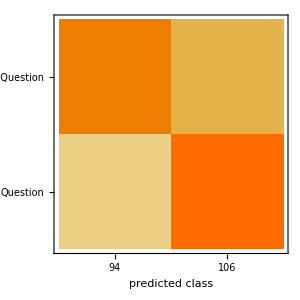

```mathematica
cm["ConfusionMatrixPlot"]
```

#### WH questions parameter

#### Improving a model and adding a feature extractor

Increased Markov Chain (Model class probabilities using the n-gram frequencies of the given sequence.) to order 5 and Feature extractor set to SegmentedWords

```mathematica
questionslist1= ToLowerCase[questionslist]
```

{she okay.,you know how sometimes you just become this persona.,and you don't know how to quit.,like my fear of wearing pastels.,what good stuff.,19643,well what's the point of waiting.,it's sixth century b.c.  do you like the period.,dance.,okay.,what are you going to do.}
 |  |  |  |

```mathematica
normalLines1=ToLowerCase[normalLines]
```

{aaa!,aaaaaaaaaa!,aaagh!,aaahghhh!,aaaww shit!...,aah!,a b...,a b-24 liberator.,64118,zeke.,zerelda did.,zerelda it's no coincidence.,zero...,zero distortion sir.,zod.,zoe come say hello to your father..,zor-el but what can you a mere girl- superman will return it.}
 |  |  |  |

Random Sample

```mathematica
SeedRandom[1234];trainquestions1=RandomSample[questionslist1,13757]
```

{did ya get the license number.,you gonna pull.,we've known debbie what since the eighth grade.,joyce give the assistant chief inspector a drink would you.,13749,miss wollsten shares the room with you.,what do you want to know evan.,will these boards hold.,like my fear of wearing pastels.}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions1=RandomSample[normalLines1,13757]
```

{when he shot up that stranger instead.,it's about to be a broken face.,a cheap trick.,i fired her damn it!,13749,a compound organic-metallic alloy.,he saw you moving yours.,well lucy it's nice to see you're feeling better.,you.92d me amazed at how many of us there are out there.}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq1=RandomSample[Complement[questionslist1,trainquestions1],1000]
```

{how is gregor.,don't you think i know it.,miller no.,you get nothing hank okay.,how do you know how bad it was.,did i ever tell you i hate costume parties.,then i think maybe i'm just a victim of movies y'know.,i've had enough good news for today don't you open your messages.,what about that rock island bastard.,were you living with miguel alvarez in 1984 or 1985 when you had your anonymous sexual encounter in the porn theater.,bree what's actually happened.,and how do they explain your status to the client for chrissake.,what did you call me.,by examining the evidence from one case we might shed some small ray of light on the other.,did it.,how can he not have a heartbeat.,you're her boyfriend.,where is that.,putty.,why did he try to kill me.,like korben can i have 30 seconds of your time here.,well what have you got.,can i taste it.,what's funny.,but you didn't see it right.,do you believe that the world is coming to an end.,isn't it ridiculous.,are we here.,you're not allowed to speak remember.,who's next.,where's the name sheet.,no more questions.,where's the polk.,you and mel gordon.,nada huh.,who fuckin' shot me!.,what do we tell him about the guns and money.,are you doing some kind of science project.,you want my desk.,what shall we call him.,but it affects my ear i don't even know if i have tmj exactly but just very tight like - it's like a muscle spasm and it's just gets so clenched -- what's that stand for.,ten thousand.,i mean two guys doing the horizontal thing.,may i ask by whom.,what's it doing on a rifle range.,damn clarice how'd you make me.,the chink huh.,take him.,joanna what the hell is-- ted when we got married it was because i was twenty-seven years old and i thought i should get married and...when i had billy it was because i thought i should have a baby...and i guess all i did was mess up my life and your life and-- ted do you love him.,what they like then.,how could you have done that.,you're trembling.,have you got transport.,are you satisfied.,permanently disrupted.,what do you think was wrong.,why should he bother us.,where'd you learn to dance like that.,would you go up please.,what kind of school.,a job.,what was your father's name.,i mean is this really gonna have to one of those big brother -- little brother you broke my gi joe and i'm still pissed games.,what would your momma think.,do. jesus christ man.,lots of people worked for her she had the business from all these retail stores.,scared.,whose blood is that jay.,so he just said --  would you dance with me.,you did this -- overnight.,does the rule of english law no longer govern.,you got money.,is mom ever coming back.,why do you shamelessly waste my time like this.,you must have upset a few people boy . . . but that isn't really my concern is it.,is detective williams in.,where'd you get that stuff.,hey but did we get to you klute.,not everybody lies you know.,well what's the point of waiting.,you have bridge here saturday.,what have you two been doin' to make it look so nice.,oh he forced you huh.,what about in the mean time.,you didn't have a choice.,am i close.,a ride.,isn't that -- extreme.,are you looking for something in particular.,so your life's not over yet right.,shall we draw up the papers or is our handshake good enough.,did pavlov condition his dogs to lick his nuts.,there was nothing.,well sampson what is it.,you mean soap.,'cause you went out the back door and nailed her girlfriend.,what is it miss vivian.,-- we can talk -- yes -- all right -- can't we talk together reasonably just -- ordinarily.,was he ill was he sick.,and you wouldn't want to explode on the basis of false data would you.,do they pay you to screw that bear.,sometimes which.,you want this guy to come home fifty years old and he's still got that little pacific stereo badge on.,what are you thinkin'.,the hypothetical temperature characterized by the absence of heat and even the slightest amount of molecular activity.,i mean what are the three terrors of the fire swamp.,what crap.,she went to florida to retire like two years ago.,we're a medical firm aren't we.,aren't you gonna get undressed.,he used that.,do you remember a miss simms.,what's he got to do with your body.,i take the man out of argentina - and it was no picnic finding him y'know.,you mean that load of passengers.,for going to school.,could it be intelligent.,well what's the need anyway.,hawkins.,my man how you doing.,north.,you think i'd be working if i had money.,j what's going on out there.,who can play god.,and if you just happen to wash out i won't have to contend with you bitchin' to some hairy-chested female senator.,i just got out of bed and you're telling me you're giving me a goddamn speeding ticket.,what're you jaw-jackin' about.,mrs. kramer did you ever work in a job while you were married to your ex-husband.,a tooth.,who the hell is jimmy.,you have eastern european girl.,do you remember when we met at the bar. ...you were wearing a tuxedo.,this the guy.,maybe see where you grew up-- did you come here to tell me how to run my business.,should i be.,you worried she'll use me against you.,killaine's wise to what.,rose, rose, rose, you poor miserable little child, don't you know i love you.,it was just a matter of time till somebody fragged his ass and you know what.,did you tell joanna she should leave me.,did i request thee maker from my clay to mould me man. did i solicit thee from darkness to promote me.,fuck what the fuck is going on -- just safety your shit and get behind me okay.,so what are you gonna do.,but do you.!,is there anything we can do for you.,did you sleep well.,they hack into people's programs.,got yourself up.,what's in sandusky.,are the girls in bed.,andy do you know who reps kronos inc..,did you see what god just did to us.,where's clifford.,doesn't that make it our time.,no. 'didn't mention he was going to the justice department.,but what if that doesn't happen.,yeah who's this.,what is love.,ready uncle lex.,this is one of those interrogation tricks isn't it.,what's wrong kittle.,do you see me talkin'.,would you relax please.,what'd i say.,you think he's gonna be thinkin' about you.,who is on this committee.,and yet you chose to leave him.,guess who's here.,what do you expect.,and the golf shoes.,go over to her place and kick in the door.,you doin' any good.,isn't that true ilsa.,what the hell are you doing.!,how 'bout the sheriff.,how can they arrest future man.,were you adopted bob.,do you think if something happened it happened there.,which parts.,who's with me.,who's the other woman.,we don't wanna be alone forever do we.,are they lying.,better late than never right.,heehaw.,and an insurance pro.,but when you first came to casablanca i thought -- well what makes you think i haven't.,it's exactly... ...you wearing a watch father.,the sky.,how can this be.,sixpack.,what the fuck are you gonna do about it dickhead.,everybody savvy.,you love me.,you say asia can be found by sailing west.,why do you think they let us in on the deal.,what you got there - beers.,profit from major sales push -- minus .347.,what is the danger.,see-- this is what we do.,you've really got it all worked out haven't you.,first paycheck.,give a guy a break will you.,why can't he marry us on the train.,vhere....,how'd you get a tux at the last minute.,homer i'll see you tomorrow.,as an irredeemable criminal.,didn't you study six-dimensional geometry in school.,all in yellow.,like who, mr. chrislam.,you're having the best time of your life aren't you.,no no the grade...the grade that you're in.,so. not bored yet.,do they know yet.,don't you see a pattern here spuds makenzie.,wolfi who gave you this.,don't we.,can you assist.,you say to me boys.,what'd you say. ...screw you.,am i right leon.,remember that corpse washed up on huntington beach.,but you <u>were</u> having anonymous sex in porno theaters in 1984 and 1985.,what an important cause he's fighting for.,six people mutilated.,do i!.,what is money.,you mean you couldn't.,you don't want to say hi to your father.,mr. barton do you remember me.,i haven't by any chance grown on you have i.,you really want to make banal chit- chat like that now.,did you order our houses burned down.,any word back from the e.r.s.,you're not going to bust out baby oil and start rubbing me down or anything are you.,so tell me something where's the flaw in that.,looks like things worked out tonight huh.,haven't we honey.,must run in the family--you wouldn't be runnin' numbers out of this club now would you son.,how do i tell them that because of the unfreezing process i have no inner monologue.,you know that first day when i come and he said i looked graceful like a capital letter s and called me rosebud.,victor laszlo.,what does that tell you about the navy.,hey bad throat huh j-man.,what do you think i'm doing.,joey dorsey.,you mean that old woman i saw sittin' in the window wasn't norman bates' mother.,who were these people.,hello pinback are you there.,i mean bad.,don't you know any other adjectives.,you're saying one of those things lays all the eggs.,so i bring some cheese.,tomorrow is the day and mum seems to be the word and i can't have that now can i chris.,what is wrong with you. ...yah -- well at least y'know i got to perform.,me. am i.,'bout what.,taffey lewis.,which one pulled the trigger.,you come here.,know what i love about dynamite.,everything ok.,then it's war.,are you a fag.,see.  it's simple.,no calls.,tick- tock tick-tock how long till your witnesses fly the coop.,how'd you find me here.,listen you still want to go girl hunting tonight.,okay what happened right before he disappeared.,then you have some hot tea.,excuse me would you mind telling me what the hell i'm doing here.,trubshaw again.,can you forgive me for my wasted life.,done much shooting with that rifle yet.,what's the temperature now.,johnny.,sergeant.,for real.,i wanna see this...where is he do you know.,you don't see that.!,where do we start looking for this guy.,how are you dealing with it.,i made her feel guilty this morning --  brother what are you doing up.,did she tell you we had sex together.,whose dreams seem to be your dreams.,should call first you know.,i can't  clark already asked me.  didn't you.,so. joanie orozco's telling the whole school she's like desperately in love with santo guerra.,for when i travel.,hey no kidding.,good.,how can you not understand that.,is that an innuendo miss teschmacher.,do you remember the day i came to your monastery when i was a baby.,what if i told frank that you opened me.,what sort of questions.,so is buddy on your short list.,first thing i have to ask myself is is he playing for me or is he just plain playing me.,and how much is braces.,you're telling me it doesn't get to you.,are you sure it was that.,so could you walk on water.,did you see my father.,how much oh-two do we have.,how long was that.,you've got the files.,how was your day.,already escaped once from the max-slam facility on -- we just keep him locked up forever.,our little paradise -- just made for two.,all you gotta do is fix a few things for us  and we'll do the rest see.,can i go to jail for punching a guy who's been shot.,do you think you can dissect me with this blunt little tool.,so how'd you get caught.,you and verona.,if there was any other way -- that bad.,mueller was alone in the cabin.,should.,that phone message wasn't for me was it.,you mean <u>nothing</u> is worth fighting for.,why did they kill the guys in the other two booths.,and is it true miss moritz that you love victor frankenstein.,am i like such a fellow.,could you get me superman's autograph.,how camest thou hither tell me and wherefore.,why don't we walk to my dorm.,scott.,the police would know the difference wouldn't they.,it's a trip you know.,in over your head.,do you have any questions regarding the sequel of your life.,herr mozart what brings you here.,is he your husband.,he used to be a bloodhound but he's anemic -- what kind of a dog is he.,in a fire.,headquarters!.,how long i been out.,well i'm not smoking okay.,what's a buzzer.,i said did you really do this just today.,how about ann.,what is your will.,snappy name huh.,do we have enough time for a weld.,sure you wanna be havin' this conversation over the phone.,neuro charged assault model.,whatta you care.,what do you have in common.,the fuck you been doin' to me.,have you checked your platinum euridium energy shielding.,oh and could i get a quart of wild turkey two fifths of baccardi and a night's worth of ice delivered to my room please.,you gonna preach 'bout turnin' the other cheek.,evacuate manhattan.,is that your idea of a winner.,okay who.,that who.,what's he got.,me.  you're the one who tried to rip off this piece.,bunny you--uhm--you on that same medication.,justice.,what's the tv say.,have you seen a lot of movies here.,well he's the one shooting up all his guys right.,you going to have the time.,no what's wrong.,so it could have been neither of them.,do you understand what i just said.,decontamination -- .,could you not take some occasion without giving.,did you come here with wally--to *not* watch movies.,when is it finally going to come out that you were the one who killed him.,can those cops down there handle dr. lecter.,can you put men at all four.,why the two extra victims.,say who.,then why don't you take the job that louie netz offered you at boeing.,what's the running time.,about my blood work.,when did anyone on that paper give a damn about workers rights.,it is evil who stands here.,you married.,what was the warning of the thirteenth dalai lama.,cool.,why what is tybalt.,clean the slut up take her out huh.!,something bugging you.,quite sure you had no motive.,any sign of the goddess barrington.,you and your brother fighting fires together helluva image isn't it.,yes mum. and something to sharpen them with.,do me another favor. ...,others.,that your heart was broken.,made your million yet.,who are you please.,was it twelve o'clock.,you been with a girl ever.,why not against your religion.,then why weep for him.,you don't think....,so. what then.,how could you not *care* about the movie.,what did you say about a pet shop. ...what.,does he treat you fairly.,what's the matter baby.,we scared each other pretty good didn't we.,is her husband sick or something.,utah you copy bruddah.,that's so typical isn't it.,i hope.,it's not west is it.,i need your advice .97.97 something has happened .97.97 mr.  jacks .97.97 why don't you stay here tonight.,how much time have i got.,can i enter.,oh yes mr. klute -- won't you both join me.,just what would you like to know inspector.,are you there.,look if there was even one chance in a million it'd work wouldn't you want to try.,aren't you being just a little harsh mothershead.,resistance.,mademoiselle you are in rick's and rick is -- rick.,you don't swing.,frank gone.,that's what you need isn't it.,never been to maine before.,bonanza jellybean.,you two come together.,know any other languages.,of what sort.,me. bob.,so you don't believe his condition is the result of anything supernatural.,what are you doing herr director.,typhoon.,i'll think about it okay.,how else do you meet them.,you'd die for them.,and while they're burning up they're still goin' down on each other.,want a beer.,who did he go to meet.,i didn't kill him -- what happened to degrees.,another one.,you know how i spent last weekend.,how much will it be with my car....,bit of a pervert eh.,where's west's body.,are you mad.,have you done this sort of thing before.,blizzards in summer.,and you can see how you feel about me right.,would you like me to be there tomorrow.,and i don't want everyone thinking i've got tapeworms coming out of my ass or something okay.,how is your pretty wife.,what about jill.,you interested in a little work.,how's the new job.,translators.,why do you interfere with my little romances.,how could you be interested in that puny little girl.,and it's not real and you don't have to even like them -- you can even hate them it's all right it safe -- you know.,what and i care.,what if it's not bullshit.,isn't it due next week.,negotiation.,can i do something for you.,you're crawling around like a-- what are <u>you</u> doing.,they are.,if you don't want to be so appealing why did you touch the rose to your skin.,did you know that liz and i got into an argument the night she was killed.,where's my share.,dr. niko topopolosis.,when will you stop.,whatever's out there <u>did</u> flip over a canoe-- i beg your pardon.,strange voices rose.,you call the sheriff on that.,how about taking to uncle larry into the old firm.,when will strader return.,y'ever smoke any shit.,what makes you cry.,what the fuck are you.,we gonna crash.,it's not your given name right.,would you like one.,do you dream.,jesus christ jack don't you see that.,it's not too cold for you mr. penfield.,where the hell are you taking us anyway.,what are you reading.,if you knew it was impossible then why'd you waste my time.,whatta ya think that outfit cost.,could you have pulled that 210-pound man clear lieutenant.,and isn't there a movie in the works about you.,get what.,when will the stream be aweary of flowing under my eye.,do you really think i'm mad.,you ever think of getting a new car wade.,and do you amuse the guests.,do we know it's him using the beacon.,i haven't got the money so what are you gonna do about it.,what dead.,so mentally ill.,you miss it don't you jesse.,hear what.,what do you think it means.,why are you always leaving me harry.,no you're going to get kissed i know i'm going to get rapped in the mouth for saying this but so what.,you have a vacancy.,what is its antidote.,i mean do you want me to go.,does she have a lover.,what he said on the phone isn't important is it.,keep your chin up and your music down alright.,i am assuming you knew these two guys from before huh.,why didn't i just say something a year and a half ago.,moscow.,here wh-wh-what.,can't i just go with you guys.,what did you hear.,without her sensing anything.,what the hell's the matter with you jackson.,what the devil.,what's going on between you two.,elevated.,i have to go i don't have time and i have more drinking to do before i go march -- did you tell her.,does it float.,when will the wind be aweary of blowing over the sky.,am i going to england.,how're you gonna hide from a guy like that leave the planet.,you gonna make me finish that puzzle by myself or what.,he owned the colored roadhouse before big o-- bledso i told the story enough times--hell we were just in the car he was stewing about the fight with buddy while we drove over to roderick bledsoe's-- you don't remember anything else from that last night you saw him do you.,westley what about the r.o.u.s.'s.,or shall i come to you at evening mass.,you going rogue on me.,did you love your husband before you married.,and that's the job.,who wrote this!.,have you looked.,destroy your career over an issue of pride.,does it.,what's april 16th.,did you get it.  did you get his money dad.,don't you know this is exactly the kind of bullshit that makes people hate you guys.,whom have i been harboring in my house.,think a soul could get lost there.,how're you doing.,we drinkin' buddies now.,so how was the concert.,what was he after.,no of course not silly -- i mean felt like this about them.,what are you trying to do to me.,are you related.,what're we going to do.,will you give me a break.,do you understand the cards.,a soul's search: finding your true calling - are you reading this.,the deal.,should i get dressed up or -- .,so. i don't believe it.,what family.,why can't we pick up his signal.,disintegrated.,grounded for the rest of the year.,but what could i do.,and that's it.,danny it's really pains me to have to tell you this but do you remember domingo that wetback you helped us put away for trafficking a few months back.,la conner.,how 'bout a cut in your gut.,is she the kid you're gonna save from the burning building.,you like telephones.,do you wish him to be amongst us.,it's all over talk about what patrick.,i suppose you want me to fix that up for you too eh.,--<u>who</u> <u>is</u> <u>he</u>.,how much money can you lend me.,how could it not excellency.,he say anything about the summons i tried to give him.,what about luther.,anybody else have an idea.,filling in mother nature's blind spots ... .,supergirl.,the question's just been where to draw it bird flying south-you think he sees that line.,why's he called 'invisible'.,is that true or pretend.,jealous of what.,why didn't you mention it in your letters.,why waldman.,what's with the dip.,patty.,was she a great fat person.,but it wasn't all bad was it.,y'know what.,do you want to come to my apartment or not.,why can't you see my side.,why did you wait so long.,i mean i owe you one you know.,your birthday celebration your majesty.,turkish.,you think i got it.,why does that sound silly.,hey what do you think you're doing.,what goofy idea have you got now.,you're accusing mrs. peel of killing her own husband.,did he not already try to convince the king of portugal of his absurd notions.,why what do you mean dear.,i beg your pardon, epi-zoo-tics.,if you're up to it i've got us set up in a suite upstairs -- are we gonna tape some stuff now.,are you there hello.,we're supposed to be different right.,who's handling the scene here.,old howard winton's cub.,what do you know.,you mind punching a hole in the floor.,relaxed.,after that ass-whipping you gave me.,shall i be married then tomorrow morning.,valentin.,why do you do this to me.,should we scramble tachq for an intercept.,you still wake up sometimes don't you.,you guy's pretty good.,is that like us.,that's desertion right.,whose childhood friends were these.,how many could you handle.,how close did you get to that thing.,isn't that your jacket.,the navy.,yes mr. poe.,what is that thing.,wouldn't you rather know.,can you accept this mission and keep it private.,geoff.!,so tomorrow between 5 and 7 give yourself a hand that clear pal.,now where is that secret knot.,how much did you say it was tom.,explanation. ...,then who changed it.,what baby are you speaking about.,playing hooky again.,so me.,machine's in.,how did the rabbits kill him.,what is this herr chamberlain.,how you holding up wade.,oh what's that.,dorothy vallens.,what did i do last night alex.,i mean depends on -- would you have shot if it was a man.,well what was yours.,so what's your point.,toughened your nipples, didn't it....,who'd steal her body.,they killed some people didn't they.,you're a butcher.,get my crewies buried.,who do you see.,are you so hot.,i guess i was wrong -- phenomenal at taking bribes right.,m436  u6563 u6568 u6563 u6563 u6568 u6563 u6563 u6568 u6568  l377510 l377497 l377496 l377495 l377494 l377493    * sometimes you stop taking his calls so    u6563      * why not.,who *live* here in this cider house peaches.,whatcha doing in the underworld taylor.,that is simple isn't it.,find a lawyer.,y'see i didn't make her feel ok about that....i would say how many men you been with.,this look like a fucking post office to you.,a shower!.,so -- which dakota you from.,do you have a phone we might use.,who is he aramis.,should i give it more time.,lex am i gonna have to lock you in the trunk till we reach detroit.,your dad play.,but you hate joey he was like a total babe why.,that's pat verona.,why can't you give me your confidence.,and why do i think they're looking for you.,is he chasing us.,riddick please! riddick.,you got a problem with me.,do you remember the detonation time.,do you need a police escort starling.,and you are.,eve.!,truthfully.,what time did he say to be here.,buy you a drink.,honest.,what if i didn't miss.,will you hold still.,come on where's your pioneer spirit.,i mean what are you going to do about billy.,can you get this suitcase to her parents if you think it's appropriate.,i don't wanna sound paranoid or like a pig but what're the chances.,where's my wallet.,so what are these spanish guys like.,i don't get off and then -- eight o'clock.,think about what.,: what are you up to.,how long for.,you never heard of me did you.,so where do you go from here.,hey we can leave together can't we.,i'm a what.,tell me when we searched the place where were they.,did you say dude finlay.,who taught you be be a nurse.,can you think of a better reason.,while you were employed at wyant wheeler you did everything you could to make sure no one knew you were an active homosexual correct.,had goodness made me a good composer.,is that what makes it so delicious.,dunbar was running out the door.,but what reason could he have.,why don't you call the cops.,are you in trouble son.! ...and his church group have volunteered to help us bring the supplies down.,have you ever made love to a chigro.,claire.,you see the bullet.,what're your taking down.,what changed.,or this side.,with all this in mind mr. kross i can't logically make a formal bid on your company can i.,rehab.,which is it.,can i see him.,did andrew beckett say i might not be able to serve our clients to the <u>best of my ability</u>.,what about the money.,i mean no one's dealing with the homicide squad yet or anything right.,little guy's getting' hassled huh.,what does charlie mean.,before or after the explosion.,can someone call an ambulance.,elaine what's going on.,-- -- who.,are you yet breathing.,now can you help me find the complaint.,is she always like this.,you wanna be a big deal don't you.,did we tape the duke game.,what's the matter matt.,keep talking to that state trooper so he doesn't notice where i'm going okay.,why should she.,how big do the bears get.,you know each other.,know but.97 you.,we all set.,uh doc i was wondering if uh this evening i could come by.,you were smoking.,don't you have enough blood already.,you wanted to see me sir.,isn't mr. lowery back from lunch.,you looking for that place in the hall of fame.,can't you just force yourself awake.,such as....,i put like this techno beat on this japanese folk tune -- wanna hear it.,who is they.,how'd ya get him in here in the first place.,you do. ...no...no goddamn use.,staedert do you read me.,she figures they'll be so relieved i'm a man-- you met her family.,are these our two stars sitting here in front of my nose.,is that the manager.,have i ever told you about her.,are you sure this is a good idea.,you mean you haven't been able to get anyone at the base for ten days.,did you get a report from the m.e..,where'd you learn to do this.,convenient isn't it.,what is it they call you.,whatta you think.,is it like that with your counselor.,what'd you find kathy.,what's the problem officer.,numbers four and twelve directly into the nervous system.,make anyone cry today.,what's the matter with them.,where did you see her.,aren't you supposed to be buried in new york someplace.,reed what if we got these gifts for a reason.,have you ever been to bed with anyone else.,i've no choice but why risk yourself.,oh i suppose you is a doctor homer.,did you get fired again.,is he a fireman.,can you stay for a while.,raban did you say.,hey -- did these guys teach you to talk dirty.,does that check out down there.,state trooper.,you were able to arrange everything.,ya puttin' me on.,jack isn't that fred bliffert over there in the blue turtleneck.,yes . . . and is there something else you want to say.,which would mean lots of those parasites right.,you mean that you can't come here and i can't go there.,are you not feeling well.,now just relax okay.,guilty until proven innocent.,i'm of the opinion that these mutants will eventually kill each other off and then-- for how long.,you like me.,i've known him for years but he ripped us off -- and you know what that means, right.,do you want her to be unnatural.,them hands you got they know what they're doin'-- ain't that right.,me.,'bout not touching the switch.,does he wear pants this color.,next saturday.,just run now.,do you remember the last time you saw him.,it's sixth century b.c.  do you like the period.,is this your idea of humor my friend.,one: how did a celebrated life of the mind bring me  to this particular switching station.,what're you -- what.,we're going to give him the money back.,you wanna do what you do it's not a crime. ...you got my e-mail.,if i risk my neck for you will i get a chance to kill englishmen.,whatever made you want to do a tour down here.,you were holding it upside down weren't you.,how long have you been playing fraulein.,who had tank duty.,what flickering light.,i thought all our colonial scouts were in the militia.,go out the way you came in.,so what's the biggest.,who's frank.,-- ok.,-- the hotel -- how far.,i mean i mean i mean why did i fall <u>at all</u>.,don't this place look like home.,how do you feel jack.,she up for this.,which one is mantan again.,everybody go it.,it's friday do you have a date tonight.,how do you think she got the job in the first place.,baby crocs.,you've sacrificed.,what about your work.,you see a couple of minors come in.,and you're not.,did you notice the beaut that came in today.,what pate.,so...there's nothing you can tell me about paul owen.,good paulie.,ain't jemima on the pancake box.,but come on harry; what's the real reason.,you enjoy it.,does that help.,i'm not gonna let that bastard take my money double or nothing.,do i seem jumpy.,what are your plans.,why does she keep repeating the name.,why should it.,he was a year ahead of us.,or now.,provided that they can be assured of her ladyship's freewill.,is everything nice but not too nice.,syevodnya syevodnya.,any further thoughts on the subject.,did you hear about that prison riot last week.,the odessa dunk.,you mean in turkey.,right now.,what's that you got there, buddy.,fry.,take your ground grogan -- twelve paces i suppose.,i endured that as long as i could do you see.,more than three less than thirty- three--permanently.,then why doesn't he simply appoint me to the post.,you remember that.,may i talk to you.,how much did they cost.,braces.,does this have something to do with that man you saw.,can we just lie and talk huh.,how is it back there.,i'm just sixteen you know.,why do my joints still ache.,can you get him out of it eddie.,pick me up.,any questions.,well jesus that wasn't so bad was it.,then you knew of the inheritance.,... coming with me tomorrow.,do you think everyone that came back would be like gus.,brother and sister still.,you just drove by it. ...for three years.,to kill me.,what time did you make it for.,mrs. kramer do you love your child.,you want unpleasant.,real.,would it really put you out if they tossed that on the grill for a minute or two.,yes....,what should i know.,are you saying that someone is paying you to be our maid and doesn't want us to know who he is.,what's going on jim.,how's he doing it.,i should have called -- how are you.,you gonna steal my truck.,and who are you.,and who else but jellybean's wild cunts could possibly conceive of doing something so diabolical as to tamper with the last flock of some nearly extinct birds.,is this paper even good.,is miss dugan well.,who is to say our morals are better than hers.,i didn't bring any  -- your volcano chum.,you always been this selfish.,neptune.,so where is it.,is he handsome.,capillary dilation of the so-called blush response.,you believe him.,when's the next jumbo.,what do you mean me.,time to change numbers again.,big on the musical comedy huh.,why do you want to know.,what do you think of her honey.,ride a thresher.,so adam...where on earth are you from.,if you were the president wouldn't that put a little piss in your shoes.,where is vanessa by the way.,then why'd we tie him up.,the milkmaid's daughter.,the medicine.,i had to tell you right.,whatiya say we just enjoy the evening.,your doctor.,do you bite your thumb at us.,why should the truth upset you.,ah stephen that's what this is really about isn't it.,are there lots of uh rugs pieces of art stereo equipment uh furniture a lot of things bought with cash.,you mean a farm.,then what do you want.,are you sure. ...he's pregnant.,but -- doesn't god ordain both pope and king.,does it bother you to hear.,did you throw away those fries hamilton.,are you married.,are we safe.,what are you doin' buddy looking for a raise.,no they don't do they.,you know everything don't you.,mr. kent could i ask you something.,who knows more about maureen prescott than her own daughter.,don't remember what day that was do you.,you got her warmed.,what's happened.,why on earth do you say that.,know who i am jake.,is that woman a complete fruit-loop or is it just me.,you here again like an evil spirit to mar my happiness.,has the response picked up.,funny how things turn out isn't it.,where's the fuckin' beer.,oh well then i'm sure that's it he got killed by a dinosaur anything else.,do you have mrs. george for english.,oh excellency would you.,where's leeloo.,mmm. would you get me another half a-cup of coffee dear.,why didn't you warn them.,could we keep in touch.,what will i say when she comes to the door.,not much point to this is there.,you mean twombley.,what do i do if i'm not that.,of course i'm your attorney i'll give you all the time you need at my normal rates: $45 an hour -- but you'll be wanting a cushion so why don't you just lay one of those $100 bills down there beside the radio and fuck off.,has anyone offered you anything to eat.,who's ryan.,are these the answers.,how did you know -- .,do you understand that.,why are you bothering me about this.,television.,look ted i'm the oldest whore on the beat okay.,it's getting late isn't it.,what'd i tell you.,i was wondering how do you guys go to the bathroom in that thing.,who'd want to let in all kinds of riff-raff off the streets.,under <u>water</u>.,where's your manners.,what it's broken.,cynthia's not coming.,fired.,a tenant farm.,what's your bartlett's.,wasn't it keitel.,nobody did anything.,who do you know.,do you think i'm repulsively fat.,vould you be villing to take the siegfried oath.,to a 'formal picnic'....,nice to be married isn't it.,where'd you grow up.,what music.,have ya lost it woman.,why may one ask.,how much do you make now.,what's this roger.,how would you get him on land.,si--tengo escopeto--just a shotgun-- you carryin' a firearm son.}

```mathematica
SeedRandom[1234];validationnonq1=RandomSample[Complement[normalLines1,trainnonquestions1],1000]
```

{metallic taste to it human blood.,acting.,i'm sorry everyone but given this extraordinary turn of events i think it's prudent that we cut the evening short.,shut up sir.,so i can go ahead and be a historian without feeling like a poseur.i shall be fulfilling a citizen's duty.,but you can't tell where one country begins and another ends.,but  . . .,you won't dare to interfere with me here.,bass!,now get your tail out of here and go wash those dishes, and stop crying!,therefore i shall ignore you.,all the sharks have had laser beams attached to their heads.,good evening miss.,caught some son-of-a-bitch stealing my bike.,it didn't go anywhere.,clearly he was injured and bled.,let's get ya started.,he didn't either...at first.,i didn't know what to do.,you little pissant-- there's not a soul in this county isn't sick to death of your bullshit charley.,the opportunity was there.,we must have a blow-out.,when the nurse bent over him he did this to her...,i kind of fell in love with her last night.,i don't have a desk in my room and..,mom's going to hate it.,i want to let the gas run out.,so yeah i've got the sears catalog thing going -- and the tube sock gig  that's gonna be huge.,with all she was doin'.,in a minute.,he mentioned a name at the very end.,i'm not screwing around.,old ties are hard to cut.,i suppose she addressed them to me in my real name by which i never thought to ask for them at the post office.,no you get out of here.,he'd be all right.,haircut.,bored.,babes.,oh naw.,oh there might be something stashed away for emergencies.,and i think you should talk to him.,if they could get her to give back the money..,in that case we'll need to make it a school-wide blow out.,but ah... ... after his wife left him and he was taking care of the kid on his own things started to change.,i'm not callin you big black africa.,and there may be a way.,it's a traffic thing.,the nuns got off easy.,you're right about that guy chief.,yeah i heard that.,many worthy of attention; but valuing is something more.,that's none of your bussiness. i have been a good worker a good and loyal worker for you you fucking asshole.,oh but if jan should find out!,c'mon, frank.,yes i am.,charley was one of your old-fashioned bribe-or-bullets kind of sheriffs he took a healthy bite out of whatever moved through this county.,you down with delacroix.,we recover the money in cash and let the insurance cover the corporate fraud.,sonofabitch wouldn't accept it.,if a thing's worth doing, it's worth doing right.,cold.,and this is china.,if you hadn't found it it would still be lost.,looks don't concern me maestro.,you barely know them.,and he has a really hot ass with hardly any hair on it.,logan cale.,awww-rr, buddy, come on, you know me!,i saw your car.,who cares if you're never known as the first girl in the nba.,well majesty it is only a comedy.,okay let's get down to it.,they found the drop car up on mulholland.,i hope ya trounced her a good one!,now's the hardest part, starling.,you understand that! ...,mommy and daddy named you julius.,gosh!,management were pin heads.,kramer i'm sorry.,oh all right.,i tried the hotel.,i don't scare that easily.,this is a six-shooter.,that's always a good sign.,right here baby.,pipe lines stop pipin' oil.,but that's your problem.,magicians do it for real.,stay right.,i've been better..,i'm *not* a doctor!,and in studying you must have learned that man is mortal so you would have put the poison as far from yourself as possible so i can clearly not choose the wine in front of me.,i'm having one.,louella parsons is here.,hope you're carrying some protection.,you know the guy who did the weismuller through the window -- home.,least of all me.,well he sure as fuck knew you!,steve said you were thinking of leaving.,we almost had an accident today.,god how..,i could value only someone whom i loved.,it's like i could spend my whole life thinking about it...,maureen tries her best to detach herself from the movie.,i'll use the chair here.,it's gone.,this has been one very fucked up job sam and i'm not taking any more chances on anybody..,got a cot in the back- people get afraid to go home they can spend the night.,i can't afford to make exceptions.,goddamnit joanna.,i already got that department taken care of...,i know i'm not exactly a girl scout but . . . maybe if i show him i'm trying . . . he'll like me.,it's a perfectly good car.,meaning viznick's a man who answers to no one.,but i want the fairy tale.,me and my bunch hit a dealer in the middle of a sale.,come on you're prettier than that.,no movie.,from basketball.,this is the mother of my child-- i thought you were married!,you'd better sit here and keep warm while i go for help.,l627561 l627554 l627553 l627552 l627551 l627550 l627549 l627547 l627546 l627545 l627537 l627536 l627535 l627534 l627533 l627532 l627531 l627530 l627529 l627525   l627524 l627523 l627522 l627521 l627520 l627519 l627518 l627482 l627481 l627461 l627460 l627459 l627447 l627446 l627442 l627441 l627440 l627431 l627430 l627415 l627414 l627406 l627405 l627365 l627364 l627363 l627362 l627361 l627360 l627359 l627358 l627357 l627356 l627355 l627354 l627349 l627348 l627347 l627346 l627345 l627340 l627339 l627334 l627333 l627331 l627330 l627329 l627328 l627327 l627326 l627325 l627324 l627321 l627320 l627318 l627317 l627316 l627315 l627310 l627309 l627308 l627307 l627306 l627305 l627299 l627298 l627290 l627289 l627141 l627140 l627132 l627131 l627130 l627129 l627128 l627127 l627061 l627060 l627059 l627058 l627057 l627056 l627055 l627054 l627053 l627052 l627049 l627048 l627047 l627046 l626982 l626981   m585  m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585 m585  harry simon harry simon harry simon harry simon harry simon harry simon harry simon harry simon helen voice helen voice helen helen voice helen voice helen juno juno helen juno juno helen helen juno helen juno helen juno helen simon helen simon simon helen simon simon helen simon helen simon helen simon helen simon simon * say.,it's shit.,if you're good enough to get in here and handle the gear you're good enough to know you don't need this.,in there sir.,give me another.,that's the one i'd've picked for you myself!,ask them what the candles are for.,right..,why that's the speech that lincoln made at gettysburg..,that's all she fuckin' wrote!,oh i fell on my keys.,we cannot.,like it or not this is the only oxygen for three billion kilometers.,second rank!,these observers were doing something.,hence the radiation.,goodnight little house.,i guy i know used to use it for his bigger deals.,blank faces here o'neil.,we advise identification possible.,she's in california.,you're my handsome man.,so he decided that one be put away as if he never existed.,you've had it.,but then i lost her.,i don't need this to hit the press.,yeah i know you have to work the whole time i'll probably have more fun here.,i think you've got termites in the house.,would you stop with that..,not as the baby they took away but as a man.,we've been trading off nursing you in shifts.,alright alright cut it coolio.,these aren't just..,you've had plenty of time to fix him up and he's leaving with me now.,just the facts general.,he could read people so chance had nothing to do with it.,uh...apone i want you to lay down a suppressing fire with the incinerators and fall back by squads to the apc over.,but you should check your backpack 'cause those guys like to steal shit.,aramis..,let's drop back an' boot up.,thank you royce.,we'll never finish the other three.,for whatever reasons i thought you might be more receptive.,i'm still editor of this sheet.,uncle this is that villain romeo a montague our foe.,i found one of your letters..,let go of me!,i've always hated you for that.,friends don't help other friends cheat.,i learned it from my guru the late guru shastri a chaste man who mysteriously died of a disease that had all the hallmarks of syphilis.,mr. balboa -- ...thanks.,she's afraid of the hospital.,i'm fine!,he just fell asleep.,and picture the birds doing their sex dance on tv.,she lives on the seventh floor.,and it just sends you someplace.,get to that chopper and hold it for us.,but i got a client lookin' to score some fire power.,somebody's in a vengeful smiting mood today.,it's our only chance.,he was losing weight.,just give it a try.,i just need to lay down.,conglomerates're lined up to finance the launch of the remaining satellites.,let me guess you're a...,i'm a girl who's in a jam and it's your job to keep me there.,i fear not mrs. kendal.,she's a good lady.,that was in style a couple years back man.,he's not gonna be happy.,oh those.,but there is worse.,how she treated you.,it seems right to us.,and you're a terrific chess player mr. danvers.,someone's trying to get out.,then the whack club i'm on loses three games in a row and i get blamed.,well i'm just an old dame without much time left so you'll pardon me if i jump right in here before they discontinue my blood-type.,claire used to tell me i loved the event horizon more than i loved her.,havanas.,maybe we'll come by tomorrow help you clear up or something.,i want to examine the crew.,but doctor that's an active case i'm not involved.,one cervical stabilizer two sets of dilators--douglas points.,for all they know..,anyway he was at her apartment a few hours before she was found dead.,somebody must have seen it.,they certainly take their lives in their hands.,it looks like we're following him.,we've got to get ready before he gets here.,buddy was more a part of the big picture--county political machine chamber of commerce zoning board if i kept those people happy he was pretty much on my side.,yeah i guess i'm still a little mad.,wallace has sacked york!,c'mon jimmy snap up snap up -- and the book says: we may by through with the past but the past ain't through with us.,general jim beam then.,help me.,that doesn't make any difference.,and i moved in with lydia...,no but i passed by it a couple of times.,what you saw tonight, we're not talking about a video some dentist takes home over the weekend.,but would you stake your life that's the question...,we do it the hard way.,i even had to pawn my diamond ring then.,tell them i've got my own reasons to be very interested in whomever did the job on the nuns.,i say we take off and nuke the entire site from orbit.,magua's way will bring only sadness and shame.,you're about to become the anti-christ who is born unholy and becomes the door to eternal suffering in this world.,remember a jedi's strength flows from the force.,there's food in the fridge.,i know the law.,i saw nothing.,i'm sure i must have been a great disappointment to her.,what it means in england -- and in scotland too -- is that rebels have forfeited their lands.,well i gave 'em a taste of american lead ... and i don't see 'em coming back for seconds!,i'll call my study partner.,ay me!,they couldn't go doing everything at once.,we didn't hurt him...,now look darlin' this is no time to go off into the fourth dimension.,and i suppose dr. murnau didn't die in a cave-in.,stuff like chat.,too good.,or sometimes not at all.,you won't believe it...,binoculars.,i'm stopping it - slowly.,almost through.,well don't give up now slick.,we'll just sell another baseball card.,you and your real estate.,homicide miss hearn.,it doesn't ring a bell.,i came on my own.,i happen to know that he gets ten percent.,no we got pressure from california state.,i've got a kid.,the king has mountains of gold!,fedorchuk couldn't find his ass with his hands in his back pockets.,similar but not the same.,all that you gotta be vicious stuff you filled her head with.,hardly two stories in the whole place.,don't even try to play it like you ain't a part of all this.,cici.,we got us a tent forty-two feet across eighteen feet at center hundred-and-ten foldin' chairs.,and you don't even do your own product!,but no one heard so i just stopped shouting.,wait...don't leave me in here..,i'm a little scared of storms.,john will be very excited.,a joker to the end.,the place produces nothing.,then swede and i split with the package and meet you back at the rendezvous.,yes so what.,you don't need to screw around anymore.,i used to play ball.,now - let's talk this thing over.,she uh...,like i said i was freaking out.,when i ignore you that's when you worry.,our kh-ll's took this one at 0100 hours.,i only hoped that your knowledge - oh officer starling...,don't you even think about it.,thank you!,but keitel if erik ever finds the horn resounding..,there are a lot of command ships.,taken together that's gospel.,drink heavily your feet will know what to do.,met her on the train.,aw shucks ma'am...,'my wife returns from europe tomorrow.,you'll know what to do.,bubba.,we all came from africa supposedly.,his name's jones.,i love the way you've arranged your pictures on the mantlepiece.,they're going nuts for these guys.,a good shower that's the ticket.,you send me a scrap of paper -- and we have a scrap.,i said...,good idea!,when i took off lady cosgrove there was no man of my years who looked so young as myself.,you're my conscience.,conklin had these guys wound so tight they were bound to snap.,i out that gun in my bag deliberately.,you know how like they say you save someone's life you responsible for them.,it's not enough that i succeed.,i'm not ready to grow old laz.,she was there...,you didn't listen to people.,trust your own judgment.,like i said-- this isn't my regular line of work so i'm making it up as i go.,you killed him.,you're dead you're fucking dead elias!,i've got cobbie downstairs watching the door.,you go full auto on a guy from close range you're gonna be swimming in blood.,they got all kinds of high-tech shit nowadays.,just doesn't make sense.,in case of emergency!,a walking penis capable of intelligent speech.,thanks for your help.,this used to be the main highway.,get away from me!,satan is not what you think he is.,they don't hold him for more than a day or two.,slamlight's so dim that you go and get your eyeballs taken out and shined up -- then you wind up here.,no you don't know what it is.,now here's what's goin' down.,now for the fire.,oh ... that.,yeah right!,just don't tell anyone i have a soft side.,she's perfect perfect.,prisoner discharged whereabouts now unknown.,bill -- bill -- bill is out there..,those which stir the imagination as well as the intellect.,but i'm the one in charge of her sorry ass.,give men that.,jennifer doesn't know.,i thought i should bring it to you.,back when buddy had it-- hell i'm just a jailer.,that's a disgrace the guy pulls a gun on a cop and he's out in 24 hours.,and i was wondering...if...if i could have a...,a hundred rubles st. petersburg hits 95 percent in a month.,i'm an orderly not a bleeding psychiatrist!,anything.,guard the shoreline.,they were quite insistent on this point and said they must have absolute assurance of her ladyship's perfect freewill in the transaction before they would advance a shilling of their capital.,that's very tempting but it's impossible i'm afraid.,you don't seem excited my little muffin.,get that doctor.,you know i respect that you have such faith james.,she's amazing.,sorry occupational humor.,well i was going to wait until after the inquest...,to perpetuate such creatures is to celebrate their crimes.,you know there's like this rule.,i want you to just keep that in your head.,this isn't gonna be easy.,she was a real asset.,if we act too anxious, he'll make us wait.,but maybe you better let me take over.,i figure.,the fit isn't right.,i - i really cannot do that your excellency.,then i wasn't beautiful.,that's how come i told you about it.,mr. bialystock.,if you just radio base and let them know they'll fix on that.,in twenty hours we run out of air.,i knew you were crazy.,let's have a toast.,it takes a while to figure it out.,you've got to show her respect you've got to show her that you're not like joe..,maybe she's not over it either.,we are fucking dead.,i wanted you to have it for your trip.,lord forgive me..,between the girls.,ah well i think i've found the malfunction sir.,she has other things to do, dave.,he doesn't belong on this mission.,he knew he was gonna get caught!,then he said that the world was coming to an end.,girls decide how far to let you go in the first five minutes.,mr. gorman just answer me one question..,he was pretty much dead.,i'm not good at being alone.,usual bullshit.,i can't get it until monday.,he can't handle the medicine.,well destructacon 5000 you have quite a head on your shoulders i dare to coin.,we don't know mary.,i can even stitch in a pinch wouldn't be a bad idea here.,you have to be good to do that and if you look out of a front window of the empress hotel in victoria in a few hours you can look right down on mr. brandon's boat the valkyrie.,my goodness.,but i do not see men on the end of nooses.,which reminds me i need some new kicks.,benoit a landlord...,this is no dream.,you have enough problems of your own.,it's seven o'clock and time for the news.,evidence.,it's 'till death do us part.,i think about that.,i knew her.,his parents are both at work.,you shut up.,supreme court.,i was misinformed.,i'm sure it doesn't bother you at all that it sounds like ss'ai k'ss two words in my language which mean excrement and cranium.,well i should probably get going.,god would never allow anything like that to happen.,he's trying to jog your memory.,here's some money.,i don't know newt.,you wanna have your way you take it.,you gotta make him do the start-up with teddy and me.,one country did sponsor the resolution.,you got three minutes.,he must have been a very powerful man.,this was mrs. lippman's house.,check the eyes ben.,and a model.,a few things came up.,i'm a traditional guy..,no nothing.,twelve hours!,you seek facts when it would be better to seek truth.,no don't talk like that son.,now i'm telling you again, get off my lap.,it blew up.,twenty bucks.,ok.,she isn't anybody's friend and i don't like you living with her.,gov want to leave me that one.,this has nothing to do with you.,you'll have to get right on it andy we're up against the statute of limitations.,i did...,they are under your protection.,that was before twombley was shot.,i've never worn the same pair of socks twice.,everyone's saying he's . . . dead.,deny thy father and refuse thy name; or if thou wilt not be but sworn my love and i'll no longer be a capulet.,i start fires when i'm angry.,i'm sick of working for that dickhead.,jesus mercy that's charlie higgins dave laller ...,he has educated feet.,then we shall state another time and another place.,don't fuck with me man or i'll blow you into tomorrow!,the first to touch it will be the winner.,tooling along the main drag on a saturday night in vegas, two good old boys in a fire apple red convertible...,and my does he hate us!,to tie it all in to gary.,the pitiful son of a bitch said rose was a nymphomaniac.,i think you were wearing that black dress y'know with the buttons.,please sit.,maybe they never got here.,oh christ!,christ it's oil of tansy!,jake you play the heavy rackets like that..,i'm not anxious to find out either.,the bastard deserves to die.,he could actually do musical harm to the princess!,goodnight monsieur rick.,whew!,this is adam.,i'm a ballplayer okay.,replace the king.,come on with the rest of it.,i can hit those boys from here.,i like 'em.,by the hour of nine.,we're even.,what i will do is keep names out of it till we got some answers or hit a dead end.,it means nothing.,it's their presidential suite.,i don't care if my clothes are taken seriously.,see you tomorrow night.,and he took his money with him.,here. 23rd street subway station.,listen it's not erasing.,it's isolated.,i can help with the eastern european angle.,the kind you tear up and get rid of.,i no gotta new-rosis.,all the blood money you had to move around to make this deal you got to know something.,which leads us to..,tell him if he would that would help me finish it.,they really applauded you today honey.,get me a couple juicy pictures.,i was wrong!,i haven't seen anything like this since the lina wertmuller film festival.,i don't know how to walk in heels.,it's hard to l-a-u-g-h when your father's dying.,perhaps we ought to stop now.,not every man really lives.,obviously so.,it'll be okay baby i'll hold your hand.,knows it's fatal.,but johnny...,all the pumps!,well my friend and partner was shot last night and i'm after the shitbag that did it.,god doesn't...,i left them here.,no mrs. lowood she doesn't write often.,and you want to tell me you saw norman bates' mother.,which involves you.,calvin i wish you would have at least let me do the dishes.,we must have faith.,rick i really think i'm in love.,you'll never get over it.,i just hope she isn't too much for him.,we need you to prepare a detailed briefing on the ship's systems for the salvage crew..,oh but i just told you.,in other words the whole goddamn world knows you're here!,myra.,nix has got to have a weak spot.,i hate her guts the bitch.,like you said mr. deckard a machine can be a hazard.,go high in the ceiling.,smells things that ain't there.,don't blow your nose!,just squeeze.,we'll find out when it goes bad.,nobody gets invited to clark brandon's parties.,i was a sorority slut.,my secret lover.,you have no idea how awful it is to be mean all the time.,i don't know...unsure.,there is a price to all this required both by longshanks and our nobles.,it's a joke.,he hasn't used any of them.,bunch of goddamn adrenaline junkies.,i won't have him back.,here follow me.,you people knew this ship wasn't ready to fly.,yes, now i'm remembering very clearly because i'm picturing.,killaine's wise.,let's...,i was recommended.,that arm you got'll get'chu on a box of cereal...,i wanted to come here.,listen the last time i admitted to a woman i loved her ...,i was sure you'd  l377601 l377600 l377599 l377598 l377597 l377596  u6563  u6568   m436  m436 l377590    teddy leonard teddy leonard teddy leonard teddy leonard     * like you've told yourself.,it's a real good chocolate cake.,i'll make a deal with you!,we've made some amazing strides in digital convergence.,well there it is.,thought i'd kill two birds with one stone.,but that's cheating!,i thought that earlier in the diner.,joel come here.,all right thanks to her and thanks to this case of epizootics you are getting another chance.,being his son all you had to do was breathe to graduate here.,let her know.,i was exhausted and could search no longer.,richard dear i'll go with you any place.,i don't think i'll be having sex ever again.,anatomy.,for most girls seeing the bolshoi ballet would be the experience of a lifetime.,true story.,how many times....it's ok...just say...,if the company felt that you or your crew were in any danger we would authorize an immediate emergency pickup.,look ma no wires.,they also found my two beam scale in the garage.,'start-up not 50 miles from here.,the night we had together..,i took one lamb.,i can zap a thousand chernobyls into the air.,you and i both know sometimes, not often, but sometimes there's real reasons why a kid'll run.,don't talk to me about elaine.,i mean if anything happened to me he'd be okay with you.,mio caro adone.,tom the fatter you get the sadder you get.,they put butter on everything.,i chant.,our paths through life must be righteous.,i am one lucky guy.,oh and make sure they send a helo with a winch -- door's blocked by a reef.,and i don't want you here.,and what you're into i'm into.,no but he heard firing just east less that a kilometer.,last time they won dr. j. was a nurse.,yeah you had a piece of pussy on a plate in front of you you'd probably kill it.,maybe we should call the coast guard.,i don't know nothing about it.,there's two cops outside that want to ask you about this -- i'm a little busy right now -- investigator...,you are home.,-- you should meet my father.,two in the back of the head.,it's only a physical problem.,let's go!,i wish you wouldn't pick on rose and tease her like that.,when i was sittin' behind a desk in washington it made sense somehow.,she sings little peasant songs quite nicely -- a completely untrained voice of course.,call me tomorrow.,skull was intact no soft tissue left--not much to go on.,i daydream.,the book again.,please don't jump on me.,we're just walking ghosts to her.,all this traffic new buildings prosperity..,and a lot curious.,oh your excellency i don't know what to say.,it's only majestic from here.,gee.,inside there's a silvery ring..,and i understand why you might want to think he could.,you never gave up.,my spouse's brother is one.,when i used to have nightmares.,that's not a spear.,i don't understand it.,what're you implying.,right in front of us.,this is not good place to stop.,doesn't want to mention her name.,she was seen leaving town in her car.,it's gonna be gone soon.,but when he tries to rescue a woman he's gone soft.,you don't work for interpol sam.,it's a rob roy.,if you know a way out of this place and you're holding out -- easy.,he has managed to alienate practically the whole of vienna.,coppery.,that's fucked it.,you look frightened.,i have hurt your feelings.,what happened today's just the beginning.,oh i do...,thought you might be interested.,well you don't have to be so dramatic about it.,i noticed your hair.,semen.,i'm plagued with my share of difficulties just at the moment.,help jamey look.,practice is only on mondays and wednesdays so...,start over with a clean slate.,other than that ask what you wish.,dave schapiro is no horse doctor and rose has been a good wife to him for a long time.,angelo we gotta talk.,just get in yours!,that's the old rick!,hammond.,i think she was crying..,now she can return the compliment.,we don't get the power back our air's gonna go bad.,poor man.,papa's right - i should put a padlock on my mouth.,yoda i must know.,the date's not set yet.,i didn't recognize you.,let's waste him.,honey this is my son delmore.,don't worry she'll tell the face to beat it.,and make the huron great.,but you can't forgive for liz.  no one can.,but no, you can't be sure about a thing like that.,the car seat that's one thing.,i'm not going anywhere.,and i didn't like that man.,i've slept enough.,opening pod bay doors.,gonna suffer you like jesus say to the faithless and the perverse generation.,okay i guess.,your husband on the other hand...,so have you.,i'm just procrastinating.,it's how i make money.,father's looking for you.,and i'm not young anymore.,back!,he got what he deserved.,well of course she feeds me.,they got it shoved in their back door.,that's what *i'd* come here for.,i want a guy like you for real.,three four.,i don't think it's gonna matter.,you'll probably squeak by.,get up!,firemen don't carry guns.,i was a hostess at this club your daddy was performing and i had never laughed so hard in my life.,no it's different honey.,alma i think there's some dirty business going on in this town.,i know he's at work tonight.,within a minute harry lost his temper and reached for the nearest thing at hand which happened to be a fifteen-inch black rubber cock.,yeah but come on...,it's got him.,uh . . . no man.,i dreampt my lady came and found me dead and breathed such life with kisses in my lips that i revived and was an emperor.,you caught me playing hooky-- i always wondered what you mayors do when you're not cutting ribbons.,so alive and spontaneous and passionate and sensitive.,i see it before me.,doing great mom don't worry about me.,it watches you.,i'm fuckin' done.,that's some good shit.,i've never heard..,but <u>i'm</u> the messenger.,if we could just talk about boys everything would be so much easier.,there's nothing to think about!,mr. penfield.,i had nothing to do with that i tell you!,max!  and you can call me leo.,here they are.,i'm waiting for your mother.,i wonder..,that bastard.,dark valdez.,ted all i wanted to know was where-- i came home tonight.,i've seen them grow up in the community.,and that royal cousin hanged a hundred scots even women and children from the city walls.,curiosity killed the cat.,we could move on.,we'll never survive.,i want to die...,do we talk about this..,why don't you get undressed.,you don't know him.,till i found out i was wrong.,you can suck a fuck.,vacation.,if he does it's his own fault!,he was talking to me and leon about marriage.,mark it mark it!,i said goodbye to you.,-- so there were two of these explosive charges placed on the power lines.,take her.,no that's fine.,atta-go.,if you're going to be indiscreet i wish you'd be a little more discreet about it.,'cause we got more important things to do like finding out who did it.,there's some vodka in the freezer.,you'd be surprised what horrors a man is capable of.,not that interesting.,gots no intention of ending up broke.,your plane's at nine a.m.  be on it.,i asked you to keep your trap shut!,they're dead now.,plus to minus.,i'm terribly sorry.,i never thought it would end.,perhaps an arrangement can be reached.,sir we really need this job.,therapy session is over.,i scoured the city for it.,it's too erratic.,from now on no more pizza!,my wife needs space i don't know my kids ' birthdays.,time i've got plenty of.,i'm just a bit of a wreck.,you know, every pageant is special, but this one is extra-special to me.,i guess i always will be.,so you're not too different from him or the chap on the roof or tommy-baby -- mm. ezra i'm lots better than you're used to.,you look thin by the way i've mentally undressed you i can see your ribcage.,forty-two-hundred i figure.,it's soo good to see you.,cornelius..,we'll meet at debbie's tonight.,i've been looking for that thing!,you'll make it outta here.,this is hardly a time for levity.,fires the eighty-eight.,oh comme si comme ca you know...,all these years i've known you you could never wait for anything.,i just thought she might not wanna meet her maker lookin' like a cheap whore.,if you see someone who's gambled here even if it's just casually on the street you must ignore him.,i have work to do.,please don't tell mom and dad..,dr. neilsen.,you think you accomplished something...,he is the courageous captain of compliments.,to me it shows part of our history in this country a time when we were considered inferior sub-human.,you john-wilkes-booth-ed him.,thanks guys.,i want to be called fran.,go anywhere do anything.,and live with me in a storeroom behind a hardware store in fairvale.,stationary with bates' motel printed on it in case you want to make your friends back home envious...,i was just showing homer the orchards...,up to now, you've always been associated with musicals, and...,but my fears were to prove groundless for on that very night patient nature would claim her account.,i know you're probably at toby's but i'm in bed reading.,don't tell me you've changed your mind.,thinking that.,he's after your money.,let him get some sleep.,you follow directions well.,we need your expertise.,we need all the help we can get.,it's delicious i think.,not enough for you to hear what i'm sayin' you gotta understand.,but i have a couple questions that i wanna ask....,it was igor at the waxworks.,money is no object.,ugh!,i'm not really.,i hate you!,ask not for whom the telephone rings ...,i never told anyone until now.,that's...,well you lost me with the last couple of cocktail words spoken m'boy but i believe it's that sort of love.,all she wrote.,you are . . . nothing.,and..,now let's get those knees up!,and the second was from my lawyer telling me he was leaving too..,standing ovation.,foredecks.,this guy is very sharp.,no - i've got a sweet-payin' job that i'm about to lose.,i been with him all day and he loves me, i know he does, he loves me and he's going to marry met be's practi'cly ast me already!,children children!,no but i have the feeling i'm about to find out.,he's just a guy who's got a nose for this shit.,at least call!,understand the carving and you will understand the people!,it's not who i am.,not to my knowledge.,you don't choose your dreams.,kitchen. . .,i'm designated driver.,great story.,just ring linen service and ask for alice.,heading three-three-four..,i was up all night cramming for this physics test and i was putting this little baby together.,besides -- when you let the enemy think he's orchestrating the battle you're in a position of power.,but rimgale's probably going to come around to arson.,you owe me an explanation.,i can offer you god's forgiveness.,he'll double what i pay you.,now i'm free of it and i'm gonna stay that way.,until ma has you home so she can fuss over you herself she's gonna make me miserable.,you're very valuable.,they won't understand you anyway.,the decision is final.,and when you said to look for signs of aggression...,and you didn't say anything.,i'm leaving casablanca on tonight's plane the last plane.,that's easy for you to say bianca.,watch that one he's an ex-spook for sure maybe stasi maybe kgb.,these are stock certificates that we bought in your name.,anger fear aggression.,hi helen.,kept calling it murder when i did it.,you were gonna get a degree maybe somethin' in business or agriculture and you were gonna make somethin' of yourself.,i feel like such an idiot.,i think jeff bridges is getting tired.,here pick these up!,people callin' all the time.,if that's not an insult i don't know what is.,not hard to find you...just follow the chaos..,god saw to it to put you in my path.,especially for..,this fellow lives like a hermit..,no it's him!,because he knows what i know -- that american families are not prepared to put their daughters in harm's way.,i'm going back to new york in--  shit!,noooo!,it was the please that caught my memory.,welcome ten thousand times.,my leisure serves me pensive daughter now.,i can't read.,you got a deal.,snap out of it bomb.,only the heads.,problem my ass!,i'm with the l.a.p.d.,vader will destroy her.,you let him get away!,i think wally will be fine mrs. worthington--he seems indestructible to me.,he's too busy rushing off to philadelphia to make stuffy old speeches at stuffy old bankers' meetings.,he's climbing the rope.,we got a kid at tailback from down your way--outta el indio-- he never asked her.,then we will both be free.,find out who a.d. is.,but if it wasn't for dignan i probably would of died.,'night marie.,i'm different.,this night you shall behold him at our feast; read o'er the volume of young paris' face and find delight writ there with beauty's pen; this precious book of love this unbound lover to beautify him only lacks a cover:,i could tell you were sad.,yeah brothers are lined up at my locker.,it's the model you've been saving up for.,right here.,wrong answer -- dunbar's telling the truth.,more light and light more dark and dark our woes.,never saw him was your basic hit and run.,want to fry the whole goddamn world.,you cannot escape your destiny.,about a foot away.,the plans for use of the maze were not disclosed to me.,numbness.,frank ligourin.,you could still help me do that.,wouldn't dream of it sir.,please don't.,see what you don't know is you're already in the last two minutes of your life.,preferred being the geek to having to explain.,i'm a law suit.,he ruined it!,hurry the fuck up!,oh god i -- forgive me...,uh...uh..,and his 'egghead' son!,i know you're as unhappy as i am about debbie's marriage to rick.,that doesn't mean a damn thing.,you just walked through the door.,i don't know that i ever even had it to begin with.,no i mean ours motherfucker!,i like your hat.,we believe that when they die he takes their money.,that's all i wanted.,we showed our ass in texas.,oh god you don't know what you're asking.,appipulai leeloo minai..,about yourself- ah i see..,oh save it.,it's about these toys.,hey i got it!,family wants to forgive her...,follow orders.,you've got to do something special.,well ask her!,just be sure you spell my name right.,he's a fucking psycho.,we're losing pressure at 280 liters a second and our oxygen tanks are cracked.,he's out of town.,you'll tell them a simple story.,see ya around.,i couldn't do anything...always scared y'know...,i object to a cut-rate one.,so i say mush on!,it's a contract violation!,i've discovered something interesting charles.,all right enough!,picked over, ten months ago.,and if you're cute and horny..,i'm looking for -- seven years work by the finest engraver.,so did dan.,if i found jimmy hoffa on national tv, i'd still have to retire in two years.,you don't like it quit.,fuck man!,you're pretty much all healed up.,he thinks that i am a gentleman and that you are a lady!,and lo' and behold as the husband of a person's grandmother is his grandfather i mantan became my own grandfather.,i'm going to get even with you you dirty stiff!,guess i'm on a roll.,and then he spoke of a girl of surpassing beauty and faithfulness.,i'm the guy in your bed the last three months.,i think he has his own plan uncle lex.,put your hand down.,legs butt and hair.,jesse james never yelled at folk..,big o's is the only place in the county that our african american soldiers are uhm--that they feel comfortable in.,i don't know who i.97.,they could try to tranq him on land.,i'm gonna go get the money.,roll the hose.,we're here to stay.,paul wasn't into that.,half mile up, there's a clearing.,bottom line alice.,what did you really see because what you're describing is not physically possible..,put up your kickstand freak.,justin just climbed into the airlock because he felt like it.,i can see what you looked like as a kid.,but i do know.,many things my french father cannot do magua can.,my friend my best friend teddy was killed in silicon valley.,you're lazy -- that's me clifford.,you made yourself scarce you could make a lot of people happy.,think i'm gonna step in and try and see him and say something if he can...talk..,so hello.,if you really want a good dry martini..,yes quite possibly.,they disappear..,that's why we must find the nest.,but tonight -- i mean anything you want lois.,hotcha character.,i always offer to pay 'em in tacos.,curiosity or even... pleasure you mustn't -- forgive me father for i have sinned.,well it really wasn't a vacation.,i'll get a new one with the insurance money.,creed's great.,i come to turn down the bed.,then you're probably happy that you don't know who you are..,twice.,but only for the moment.,or parties.,think it through!,your legs don't look broke.,we'll go talk with anthony and figure it out.,i saw him in vegas once.,then let us try together.,they both looked mad enough to kill him...}

```mathematica
SeedRandom[1234];testq1=RandomSample[Complement[questionslist1,trainquestions1,validationq1],3600]
```

{you've been going round-the-clock.,we need to have the evidence ya know.,and the bad news.,and what am i supposed to say to the man.,how long you been working there.,what do you do and what should we call you.,do you know how we say make love.,how we doing colonel.,that spoke to you.,leaving what.,whose justice.,why'd you do that.,know what else.,how deep is the ocean.,well who was it that taught me how to do that.,good morning luv who are you on the phone with.,awake.,why should it be so.,you know who that is.,if you weren't mine you'd be someone elses correct.,look you want to make it up to your friend.,the scots will fight for us.,have a sniff of this why don't you.,who can run the estate.,then what are you doing here.,the fuck you laughin' at.,where'd twombley get shot.,what the hell you waiting for.,what did you talk about.,what about the report from an eyewitness at the liquor store who said one of the brothers was shot.,excuse me for saying this but what is wrong with you this week.,you'll back me up with some paperwork.,why are you shaking.,why do you ask that.,then how come she never said anything like that to me.,it appears to be dirty -- why don't you get somebody.,but doesn't someone taking your costume so you can't compete overrule that rule.,what do you have danny.,did you see hiromix last night dancing with bambi.,and are you afraid.,he taught all this to swann.,ma what's wrong.,shall i remain here in our hotel room hiding or shall i carry on the best i can.,how do i do that.,do you believe me.,ready to gogogo.,dartmouth.,so. old man tucker is just standing quiet outside the bank.,i mean how many plants were even back there.,are we gonna keep going with this game.,something the matter with the cuisine.,why wasn't i insulted.,missing..,anybody home.,is rose going to die.,she died.,so we got crosses covered moving right along what else.,and i hear my friend callin' for help and i look and she has falling in the water-- you have somebody else out there.,how did he know he'd get the chance.,have you seen him.,you recall if charley wade was a mason.,do you have anything derogatory to say about the champion.,morning after. ...i'm at least half a bum.,where's czech girl.,are you asking me a question.,did that thrill impress and overwhelm you.,will you join and take the bounty sir or will you be given up.,rose who were those scoundrels in birmingham.,i'm the guy who took the pictures of you and acme playin' pattycake remember.,my colors.,you don't wonder that.,have you ever had sex before.,she didn't take it from you did she.,sure evan why not.,twombley.,how is your bronchitis.,just to leave her like that.,i'm glad for the chance sir but - why me.,when you planning to cut back on that.,i just wanna deal with the boss ok.,she never gave any indication where she might go before she left.,would you like me to ask it again.,where's ronnie.,the police always do don't they.,you getting jiggy with mantan.,since you are a friend of my daughter's i think i'm entitled to call you james don't you think.,gee eddie you're not gonna go are ya.,they will send a nurse someone who can take care of all of that for you -- i just i just -- i just -- i'm just in a fucking state i know he's going and it's like i don't know how -- just tell me <u>practical</u> things -- what the fuck do i do with his body.,pittsburgh.,is it yes.,and the weed.,i am the co-ordinator in this show and you will answer the questions that i ask you understand.,is it so unbelievable they don't care about you.,what do i do dad.,me i'm kinda aggravated. ...fine. ...how's the turtle food this week.,why aren't you there right now.,can't you see that i'm at your feet.,would you just get outta here.,how was he supposed to say no to that.,how you doing man.,may i finish.,do you love me rose.,the lord bless thee and keep thee.,you got a hundred-fifty thousand dollars didn't you.,can i be excused.,how many times have you seen frank.,up here on the fifteenth floor.,what set him off.,general.,what if your girl's theory turns out to be bullshit.,what'm i gonna do with half a cent.,he's not.,were you planning on kissing me when you finished quoting.,coninued well what is it.,nobody really thinks it's going to work do they.,he can barely pick up an escort girl let alone...what was it you said he did to her.,will you men help us stop the french.,how could it be a charade.,mom i mean dad.,well what'ya do.,i'm not a doctor. ...so you feel absolutely no responsibility for killing these people.,lost in the storm.,i mean what do they actually have on future man.,it wasn't very good last night was it.,hey uh don't go freaking out on me over this but do you remember when your dad first got his video camera.,listen listen -- i can speak -- well bright eyes is our throat feeling better.,what direction does the system indicate.,what do they get.,the only woman.,you never did like me much did you verne.,wanna walk me home.,rocky do you have any representation.,so i should stay silent about his misdeeds.,you felt nothing.,won't you see me later.,she her own you know.,where's the woman.,that obvious huh.,what did vinovich say.,in that room.,what do you want from me colette.,where do i charter a boat.,about clothing.,- where that come from.,how do you know this.,now then mrs. kramer would you tell the court how long you were married.,rose are you all right.,shall i send a car.,me.  thelma i'm not hostile.,i mean what kind of people do well at this stuff.,what kind of goddamn monster are you.,what's he gonna do arrest us.,listen this girl worked in a tanning salon need i say more...,does that scare you.,nobody's asked for me have they.,then what do you suggest big shot.,you have not met a man worthy of your attention.,doolittle are you there.,how do you know my dim-witted inexperience isn't merely a subtle form of manipulation used to lower people's expectations thereby enhancing my ability to effectively maneuver within any given situation.,what are their names.,what is it the stairs.,who is that guy.,what are you going to see.,do you have any idea of what is causing this fault.,do you want something to help you sleep.,reaction to what.,vivian how much to put up with me for the entire night.,then i am going to the meeting of the -- now you finish locking up will you carl.,how can i help you mrs. peel.,radiation interference.,who'd you call on the phone back at the booking station.,you realize how rarely they make that ruling.,has that girl -- has thea ever told you where she comes from.,you want it back.,do you see them.,hey taylor you okay man.,who can we trust.,do we have news from the delegation in china.,would you prefer someone else now.,somebody..,do me.,hey what kind of talk is that.,well underdeveloped.,what deviant groups or organizations did he secretly belong to.,what counterfeit did i give you.,lay off once would you.,who will read me my stories.,whatcha doing.,block it up.!,men.  they look more like weasles to me.,what's the matter with bjorn.,and let every rag in town grab a red-hot story.,need some help.,apologize to that wimp.,do you have a note to corroborate these claims.,where is son.,cates what's the matter you been takin' dumb pills.,for the whole night.,did you have a nice swim.,isn't it true you have spent your life pretending to be something you're not so much so that the art of concealment and dishonesty has become second nature to you.,what have you got to do.,can i take you to the airport.,which way is my way.,darling where are the glasses.,you serve martinis doncha.,you think you're so god damned smart don't you.,what if there were a connection between the two.,so we're not supposed to tell anybody what nobody knows.,what are you doing ted.,you dug this up all by yourself.,rose i don't -- who.,by breaking up a company's assets -- what.,why do they have to die for me.,if his friends don't help him who is going to help him.,so why're you even considering it.,you did this.,yup you must be harry.,did you see the size of that thing's mouth.,i don't think evan gets to be in it -- evan guess what.,what do you want me to do rose tell the g7 to fuck off because i'm a family man.,he's going to take care of that mortgage for you . . . mr. dickson.,have you listened to the radio or television.,why doesn't she just hang up and call the police.,you know how i know.,i'm helpin' you huh.,suppose there's an atmosphere of some kind inside cyclops.,yeah would you hold this for me.,tough guy huh.,just stop playing with her mind you know.,why do you always answer a question with a question.,after all he is the president right.,lemme try huh.,when are you meeting the man.,is detective gordon going to be at your house.,what else my dear major.,can't i touch it a little rose -- not a lot just a little.,or the guy she works for.,call that fresh.,how do i know you didn't kill larry.,for five hundred what do i get.,what about my ship.,otis what.,boy you guys are really something y'know.,you know what gets old.,you got my check didn't you mom. it's nothing you did mom believe me.,peter where are you.,do you know what i had to go through to put this goddamn food on the goddamn table.,as it matters in battle.,if i break one you gonna shoot me.,what you gonna give it all up for a maple twist.,and why are you so glum.,for instance i have got the gout; who tends me.,you through mr. wizard.,years why.,what's going on in berlin.,i was listening -- did you listen to me.,bloom like a flower.,how many pupils do you have.,just let me walk out ok. please what is it please -- let me go leave me let me go it's ok please.,guess who mom's having dinner with tonight.,you take it straight.,do not be tellin' us what to do with ours. ... and while they are cooped up in your fort what if the french send war parties to raid their homes.,what'chu got in this.,come what says romeo.,where are you two going.,are you going to remarried phyllis.,where'd you get the blood.,stick to stuffin' the olives willya dolores.,what happens here.,safe.,if you feds are so hot for him why don't we just bring him in right now.,what are you talking about fella.,did you see the play.,you two are gonna help me tame the wild beast.,who put you up to this -- the manager.,are you sure you even packed it.,carol burnett.,why do i know that name.,what are you doing with your hands.,that the word on our boy.,that really happened.,will you buy the sheep for me.,know that.,did you ever think of that.,while you're waiting for your friend would you like to see some new figures i have downstairs.,hey do i know you.,so you decided to help him after all.,huh. ...screw you yoyo.,but -- what is he doing.,may i try it.,may i be quite frank with you.,starck you still showing those readings.,how could i be.,so you're telling me it was one guy with six guns.,do you call it a game when only one man win each time.,you're supposed to say 'colored' now right.,who was he.,when do i begin.,second why put the charge all the way down here.,chief what the fuck is this.,come on jack shall we go.!,do you have the suspect in custody.,so are you like gonna polish our nobs or what.,don't you feel anything for me at all any more.,you're not married are you.,are you gonna tell me about police procedure.,oh princess leia are you all right.,oh -- well i thought he once mentioned -- why would you suppose so.,well need i remind you of the consequences.,would you like to talk about this friend.,i coulda had my head blown off and for what.,did you do those drawings doctor.,i can see that what're they for.,hey what's with the mouth.,were there any calls.,where'd you get them.,shaw's fighting in south america -- why not postpone the bout until july fourth.,what the hell's he going to moscow for.,how can i believe that there is not a man who has inspired desires in you.,and who is that.,but not completely inconceivable.,you think for once we could talk about something besides basketball.,what exactly is this place.,i'll see ya around huh.,pay money.,when are you and matt going to get married.,does he tell him he's been giving head out back for twenty bucks a pop.,i'm...that's then what you get. ....are you still walkin' in that car....,you called me.,excuse me skipper--- what about time....,you goin' to the escort service.,this is he.,you had one guy like that.,whatsamatter.,you think magruder wants to hang beside me.,or is it disgusting for someone to take a dick into <u>their</u> mouth.,are you wet.,she triumphed over everything what are you blubbering about.,he said what.,pupils.,they always let felons sit in on honors biology.,did they tell you to sleep with me.,girl....!,i can't make a simple statement without him taking issue with it what's the matter with you.,mind if i ride along with you.,it's a college town you know.,doesn't the dream master work for you anymore.,will that help.,how much do you know about what happened to you.,how did you hurt your hand.,how ya doin' farmer.,pretty ain't it.,what's all the panic about.,when *doesn't* he have bronchitis.,'i like him'.,any bit in particular.,do you know lily.,listen stupid could i do anything that would possibly meet with your approval.,how is it you come to be here.,who is dead.,it's like a cab isn't it.,mr. dunn can i ask you a personal question.,did you keep a picture of your lover on your desk.,has mr. kessler said anything regarding the attack on the moors.,what'd ya see.,you know what i'm going to make.,are they close to catching somebody do you think.,you want me to cry on your shoulder and tell you that everything's all better now.,should we stay here.,hey 'top.'  what's the op.,that bugs you too.,are you two all right.,you want to sue wyant wheeler hellerman tetlow and brown.,if god had intended man to fly he would have given us wings.,you woke me up to tell me that.,how many questions does it usually take mr. deckard.,hey are you awake.,where's ma. you no-good pup!,drunk in a bar in mogadishu.,what do they do for you kaminski and his friends.,cash or check.,are you comfortable.,what number did you tear out.,the paperwork alone.,notice something funny about that bus.,hurry.,you mean ray dunbar.,what does that mean -- to be noble.,come on will you.,do you need a break.,well... about half an hour ago that woman from the talent department called what's her name.,how 'bout i take you home.,what is the point in that.,your junior life-saving buddy.,we gotta move -- what the fuck are you doing.,are you still with us.,yes. ....you have it...easy....you know.,what have i done.,yello.,just what are you up to.,is that how it's going to read.,you want to go outside.,why don't you come.,what is the secret of your art, plum blossom, huh.,never mind his excellency -- you gotta your pocketbook.,because i didn't grow up on food stamps and welfare.,he's in interrogation.,now i know you like him i know he's nothing like those frat kids you can't stand but honey after the excitement wears off then what huh.,you with mother or father.,i'ii go....is it...back here.,c'mon why not.,he looks great though doesn't he.,what i mean is do you really know what's going on in his head.,you ballin' her.,do you really.,ah - you've heard that.,with grenadine right.,who the hell is ron johnson.,we'll meet in three hours.,can i call you in a little while.,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person.,something's wrong.,is the hatchet buried between the english and my french father.,where on earth have you been!.,what's your name again.,yes captain.,mark are you okay.,he committed suicide.,what is it hal.,stevie.,what are you doing on the fourth floor.,how many bullets left kid.,what would you do holiness.,how the hell do you find me anyway.,are you in show business.,have they questioned you yet sid.,look butthead i'll treat you so nice you'll never want to let me go okay.,can't you take a guess.,where'd they come from.,need you my help.,what do you say to flying out and giving me a hand.,you think <u>i'm</u>...  ... gay.,how the hell are we supposed to get this donkey inside.,you do not wish to be beautiful to your king.,what is it my son.,what are they doing what's happening.,how can you even think such a thing.,bizarre small world huh.,why don't we charge them.,where do you come from marvosa.,-- hang on -- -- yeah -- one guy -- i don't think he was ready -- -- it's just him.,what the hell's wrong.,what business is you in jack.,the rest of this is all .30 caliber-- yeah.,may i.,you stopped it didn't you.,so that's all you do....,what if i chant.,is it over 'cause you're sick.,how do you figure that.,how is central these days.,but later allright.,do you want another coke stacy.,will you be getting back together.,now let me see - a half hour after the dooley sisters - and the dooley sisters never get home until after.97 what time did matt brown get in.,you came up here on a hunch miss crane.,can i be of some help.,where is your attacker.,are you busy on friday.,damone are you there.,with all due respect i told you to abort -- didn't go as planned.,it looks that way doesn't it.,how's our deal coming along.,who the fuck are you dr. joyce brothers.,you don't mind do you.,shall i ask the chief of staff to schedule your daughter in.,then what's love.,where will he go.,the one who tried to kill me.,and nobody could tell me who he was -- an exiled prince or a mercenary or a bullfighter or -- but i felt it stirring inside me this -- this wild pagan feeling -- yes.,how often does one of our clerks have business in the house of records.,will you give johns hopkins a new identity.,i'll buy ya the best dinner in san francisco...how'd that be.,do you have any coke.,do you know her.,and, who's your colorful little chum.,you wanna go on a date with me.,was it ever.,no more kids yelling 'your old man's a thieving rapist'.,and what do you do.!,how much is the lemon meringue pie.,just incidentally -- why are you wearing that.,true.,that's all you've got to say you've got a bad cold.,so my letter brought ya flying eh.,what's that a gram.,is that all you wish to tell us.,plus where's huggie bear.,you a couple of fags.,you bring the cigarettes.,you know where that kind of money comes from don't you.,when did you see the dale girl last.,is it new.,permission to leave sir.,habib.,something wrong with the stairs.,do you love victor frankenstein.,what's in the box.,a lincoln.,hey rock -- what happened.,how did you acquire a taste for it.,a man or a mouse.,you want a hit.,so...the station is empty.,so you can starve him.,i got nothing against-- you have a thing against museums.,wanna keep goin'.,you hear me private.,oh miss price.,l627077 l627075 l627074 l627073 l627072 l627071 l627068 l627067 l627066 l627065 l627041 l627040 l627020 l627019 l627018   * what's the plan.,a... human like creature.,so i'm part-indian.,max, what is it.,you knew you had a double.,and when the other rabbits hear of fiver's vision do they believe him.,oh shut up huh.,how many women have you known.,how you feeling all right.,what'd i do now.,you've heard nothing about the incident.,are there anymore.,so now where were we here.,cunningham was it.,cmoncmoncmon that one to.,without calling me.,what kinda job is it.,so who was he with.,what's debbie's blue book value right now.,why romeo art thou mad.,whoah what a day huh.,but - what can we accomplish.,you mind if i take a swim in your bathtub before i hit it.,what's your subject.,why else would they have a severed wolf's head on a spear as their symbol.,it's just i don't want to get one of these paid ladies you know.,who's camille.,tanks huh.,you want ten.,rose rose.,are you looking for love from dunwitty.,diet soda.,does anyone know his politics.,you've never heard of napoleon brandy mister smarty-pants.,why is he acting so strangely.,you been on prozac long.,mr poe.,what was i gonna say.,you don't like it do you.,has the patient in twenty-one gotten his tray yet.,and he is still willing to give you a visa.,surfer grunge hip- hop euro trash.,what if someone tries to steal it.,is it true she's never been to a dentist.,do you understand what that means.,is it fresh.,it needs blood.,jesus pop how can you stand the cold dressed like that.,how do you feel this morning.,- or anything else - would you be kind enough to call this number.,aren't you going in.,now i can't do it cause i'm tied up but we get the others to go along -- how.,why isn't he in the general ward, then.,can't you just quit.,stalling eh.,you've been here before.,what gang you talkin' about jack.,you think we forgot that.,half watch dog.,in movie they make of us who do you think would act me.,cut to int tubbs' apartment - night it's just...catching up with me you know.,fezzik are there rocks ahead.,why what sir.,don't you think they'd know that figure would be recognized.,i want you to stay -- what's this.,how much did it cost.,oh no.,what if he doesn't show up.,you know we have met already.,could don king be near.,me.  sure i do.,makes you feel small doesn't it.,what are you after pam.,what happened to them.,what kinda beer do you like.,i'm from cape town originally first visit to london.,is that the best you can do.,we wouldn't want you thinking you're the only show-off in camp would we.,yeah brother look i was calling cause -- has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley.,you're not losing your hold on him are you.,when did we get it from them.,why do you say i'm full of shit.,apone...where are your people.,what's goin' on in here lad.,what an awful thing to say and where did you get any such idea as that anyhow.,we leave in the morning.!,you made me look like an idiot -- i believe somebody owes me ten dollars -- baseball.,liar.,perhaps the police.,sir.  what did he say.,i fail to see -- the world council of ministers meets tomorrow to convene the new global defense initiative -- getting to what.,so what's unique.,hast thou not a word of joy.,is that my -- scenario.,what kind of story is this.,it was staged.,what's a tree.,stacy what are you waiting for.,are you my attorney.,who have you been talking to.,did you threaten this man or use profanity in any way.,did he not choose a carpenter's son to reveal himself to the world.,or that little guy with the glasses.,don't you wonder why i do it.,part of what.,this my shade.,you don't know who he is.,you want me to help.,what do you have here billy.,clarice....,where the fuck is she richard!.,how many wings have they got between them.,and - .,upset that i rubbed off on her.,you think god forgives people like me.,only two steps back.,and you'll join me in a sambucca.,smoke screen for what.,are you familiar with the work of aristotle.,you wanna see baby.,so when do we leave.,whose rooms are those.,you got the guts, tough guy.,don't it matter none he's makin' ya out a fool.,and then one day you wake up and say fuck him.,is there a part for me.,doctor tell me honestly what do i have to do to get out of here.,and we're sure lydia's gonna make her move.,mr. pizza.,twenty-five.,you have something dr. weir.,where's joanna.,what did i say about mentioning that bitch.,did the rancher fuck you.,what's the russian for ant.,come again skipper.,what did you tell the people.,no paris.,how long will you be.,explanation.,what are the chevalier's intentions.,is that what you're doing or are you the real mccoy.,you wanna make a deal with me.,who's lacerda, he's waiting for us in a room on the twelfth floor.,did we get our bill yet.,still need a lift.,you fucking asshole who the fuck are you.,well isn't he.,did you call.,did you know he was going to be there last night.,what the hell's it matter.,a drug counselor or a drug dealer.,went to another school you see.,we'll stop at a motel -- kate scott.,where's dad.,you want me to read this or not.,yes they do, they do, but i'll make my dreams come true, you see.,why did you keep your marriage a secret.,how you sound.,can't a boy be a dorrit.,well what shall i swear by.,you know billingsley's.,what kind of an army do you think we oughtta have.,my condition....,why don't we see what we find out from the blood work.,uh yeah coop i'm still here. ...do you copy.,right clarence.,what would happen if i knew something like that and didn't report it.,how far from here.,do you have me.,ready to stomp sod.,brad.,did you expect him to look you up.,aramis -- how is he.,your year of absence.,since what..,how come you were in my truck.,you like ceilings.,keeping a stiff upper lip.,she didn't call anyone.,all right who serves.,assault and battery.,you think i don't know what you're doing.,i made a few phone calls an' thanks to me ya goin' to be a big man -- thatta dog.,so are you like grounded because of last night or what.,can i stay.,what did your father do.,but . . . but isn't the world about to be osterized.,what was all that benevolent crap.,three years digging up worms in chernobyl.,how you holdin' up kid.,you got some business that's not exactly legal.,isn't it incredibly obvious.,is everything ready.,roddy will you see me insulted.,flea.,what do you mean sire.,where are my glasses.,hi viv.  carlos you know my roommate viv. you spent it on drugs didn't you.,a good thing, right.,the <u>winners</u>.,what if she forgets.,but why take the chance.,why not what can they do.,look you want to fit in here right.,will you get out of here you meat loaf.,which one was that.,so how long is this trip.,who's mr. jocularity.,do you really want to talk to me and say things and get things figured out jimmy.,it'll spiral in toward its sun and -- remember when the artificial gravity went out in the toilet.,why stop with just one aspect of marine life.,- for horrors like yourself.,how someone strong like you scared from a message.,why can't i go out there with you.,all this time.,does that work.,*what* view.,do you have a boyfriend.,'his' side.,you want to tell me what's going on.,what -- what do we do.,the nocturnal flying mammal.,an eccentric recluse.,and the bodies.,your base isn't secure.,what's so funny.,what about friends.,would you rather be ravished by a pirate or a british rear admiral.,another woman.,ed gein.,how does mrs. eyes only like being married to a guy on everybody's hit list.,where's the restroom.,did they look like psychos.,how'd you get this.,oh baby what's going on.,how did it come to be in your possession.,and what does jennifer think's real.,you know who i am.,what the hell is that sound.,together.,do you think that's funny.,goodness-gracious it hardly seems real y'know.,what about the other one.,well where was patrick.,you know how to fly this thing.,coming.,it's not just inner beauty is it.,then why bother curing me.,do you want to come inside.,so you want to nail the ex- presidents.,what makes you think you can order me around.,well you're the man out there now aren't you.,will you come see her with me.,who did that.,outside it's--it's such a mess--it's-- because it's a job.,a fine state of affairs -- no wonder you can't matriculate now what were you saying.,where did you get your overnight bag.,you know how sometimes you just become this persona.,and an intelligent person can make his own choice .97.97 that's it isn't it.,hast thou no letters to me from the priest.,what does thou make us minstrels.,could we interest you in someone else.,this is a club sheriff--you been in here-- what's this i see.,want another beer.,then you screwed up something like that so if you disappoint them from the start you're covered.,i'm sorry did she make it.,tecate.,why you're alive.,that's not a helluva lot is it.,disappoint me.,what are the heads.,hadn't put in a good word for you.,can i be of service miss price.,do you always drive this fast.,are you comfortable here.,do you have a cross.,this is all that survived.,remember what we found.,you do want to play.,anyway what the fuck do you care.,you're a nice guy without all the entertainment okay.,will the company put up five hundred dollars to get jane mckenna's list of clients.,dr. allen could you please tell mr. kelson what you heard as you tried to enter mr. birdson's room.,it's quiet-- we'll get 'em--  so you livin' out here now.,nothing important but may i speak to him now.,for one thing we're gonna need to turn that music down so we can talk ok.,why are these all opened.,and what was so important about it.,what game cobb...,do you want athos arrested your majesty.,a son of your own.,was god expecting me to offer forgiveness in the face of every offense no matter how painful.,me.  i don't think so.,is the dead guy in there.,when she was willing to sacrifice us all.,well if we're friends why can't we see each other.,what did it say.,the shooter knew these guys huh.,do it with all those boys and men.,are you finished with me.,you gonna give me that.,how would i remember.,everything that went before all that stuff that history--the hell with it right.,you a senior.,singed a bit were you.,how about this child.,nevertheless what'.,don't you see the opportunity that lies before you.,what's that long building over there.,because i didn't call home a cardboard box.,you just quit bein' a priest or somethin'.,did he ever fail to provide for you.,what's your favorite scary movie.,do you know where we are.,gay <u>pornographic</u> movies.,how long have you worked for the agency.,i'm not sure i hear a question in there.,and this butterfield guy-- after that fall..,what did they want with a traffic warden.,want to take a walk.,listen i hope ya don't -- yo a bad reputation -- twenty years from now people will say 'd'you remember marie.' 'no who was she.' 'she was that little whore who hung out at the atomic hoagie shop.' 'oh now i remember!'..,can't it wait then.,how 'bout some cokes.,dr. floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question.,how'd you spell that again.,questions.,wherefore art thou romeo.,what about here.,another ear.!,and you believed me.,at a time like this that's all you can think to say.,jeremiah do you realize what this means.,is it worth risking your life over ten dollars two credit cards and a lipstick.,you found anyone in yours.,to a private island like you.,you feelin' sick.,for. . . .,at any time phillippe could be discovered and what then.,the 'maze'.,please can't you help me.,do you think she'll be all right.,what was my wife doing in your apartment last night.,alright kincaid no where to.,about acting.,why do you eat that stuff.,where will my toys be.,see that.,what did you wish for honey.,stick around please.,whatta you need.,by accident.,and i suppose you see him in some sort of strapless  thing don't you.,you returned this westley to his ship.,you promise you won't tell.,why would i do that.,and you were not hurt.,i was insulted so i asked her if i was wreaking some wicked b.o. right.,is anyone else in this house right now.,you think they sold me out.,what's the occasion.,y'know -- make love.,the hell is this shit.,which is the one - we have to worry about.,this is a good level isn't it.,you give up on her.,what do you like best about her.,uh...sure...i...what.,what am i -- a security guard.,but what changed our mind.,would you like some coffee before we serve dinner.,did you use this same car applejack.,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden.,you heard of harry lonsdale.,a toy.,what you've never seen one before.,what have you got for me.,you remember margie fogg.,can you make it that far.,mother what are you sayin'.,so what dead-end street did you and shawnee hit.,you're not...an orphan are you.,you don't find that repugnant.,where is alsace.,is there some kind of expression i've picked up from beckett.,how long are you planning to stay.,how's she doing.,the irish representative.,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change.,tiring.,how long did this attack go on for.,you ever know a fella named eladio cruz.,me and alterez are on it okay.,who is pamela landy.,singapore...thing.,and what else.,how do you sign checks--.,<u>her</u>.,you going to get married.,in which part of me did this knowledge reside.,if she had what reason would she have for not calling you.,what'd i do.,he's out of prison.,justin.,professionally.,you can't say things you can't tell anyone it's like the privelage right.,how much will you pay him.,look stephen maybe we can talk about this some other -- yeah.,some tea.,you don't want to be a public nuisance do you.,by the way how're you fixed for spys.,six huh.,not yet -- give you the clue for the bust if you show me some trust -- oh you're a rapper huh.,does he have some genius stowed away.,he's a cop.,major what do you think could have done this.,patrick what's wrong.,you want to get into a finger pointing contest about character.,and jd is his dad and owns the whole property.,they wouldn't.,you want a lift.,a ride where.,jealous.,bad people.,wash it to the windows.,i believe we share an art instructor you know chastity.,with reproductions. ...do i.,now what the fuck are we supposed to do man.,and how do you feel today.,and if so which part do you think you would find the most delicious.,hey where's the fire sister.,what is the meaning of that phone call.,why don't we move on.,if - all flayed....,then again something has changed hasn't it.,don't you feel eyes moving over your body, clarice.,you people seeing the old year out.,why don't you have anything nice to tell me when you activate me.,how'd we do.,are you sure there's nothing else i can bring you.,and if i don't obey.,one of the two men was hubley right.,you're not scared are you.,oh, yeah.,so we should hang him for it.,what would you call it.,it's all about that night isn't it.,what are you asking me.,can we swing that.,what do you mean west's.,what's happening here.,dad--.,you're polish.,the blast.,how about you two hit the strip and start knocking some heads together.,do you think the police did a good job.,so you can beat him.,the safe was up on the ceiling remember.,did you know that ted bundy's first dog a collie was named lassie.,what value is that.,what happens.,-- you decided you liked it after all the other night; you'll hang around for seconds.,patrick have you ever wanted to make someone happy.,he's a guest in my house isn't he.,have they located my daughter yet.,i thought you had retired from field reporting.,how you doing down there.,how long are you here for.,is that whiskey in them glasses on the bar.,how terrible can it be.,what about the killing and looting.,what did you find out.,are you sure you want to stay.,where were you all afternoon.,what  .,what does she sell.,-- how would <u>you</u> like to be in a horrible situation like that.,you think that's a good idea.,then it's malaria.,what's that mean again.,you mean with you and that woman chained to ya radiator.,jack crawford is helping your career isn't he.,and what if i tranq him kelly.,she's alive.,not great.,yeah you don't remember.,where'd you grow up a barn.,busy when you were gone last year -- where were you.,yeah but are you crazy enough.,i'm wonderin' wether or not the weather people use outside meteorlogical services or if they have in-house instruments.,what of our marriage.,no jokes about my name.,what was the matter with it.,hey where the hell were you all day.,get some peace you know.,you ain't happy about the green light.,what has he been to me.,that makes it all the more difficult .97.97 have you any other relatives mary.,how would you like to be the only kid in town without a father.,what the hell's a freeway.,oscar what's the matter.,are you hit.,and where did he go to school.,where the hell are we going to go then billy jack!.,a girl i didn't even know.,what the hell are you doin'.,what kind of trouble.,how's the food.,freezing and wet.,you think you're the first.,is mom okay.,and the germans can't match it.,do you like me.,who me.,his father's dead right.,what you were going to come over the next day all calm and say kelly that really made me mad.,whata you mean i've got no choice.,has anyone told him we've got a dragon eating our boat.,you know - it <u>is</u>.,what if bourne didn't have anything to do with this.,you want a dressing bag john.,could these wormholes appear in nature.,is that a beastly thing to say.,will you do me a favor then.,why aren't we still following them.,what do you say sir.,what's a scam.,clockworks.,have you gone mad.,got a pencil.,c'mon you wanna sit at the grown-up table or not.,-- fezzik please -- his true love is marrying another tonight so who else has cause for ultimate suffering.,have you written that name down.,who are you sirrah.,witchcraft.,did you really think you were slick enough to pull this off.,is there a problem.,anybody see my boy.,why wasn't this patient properly admitted, and why is he in isolation.,captain miller you copy.,philip swann.,ring.,would you like some money.,hey don't you think a hair stylists got any interest in gettin' it on.,who's the father.,do you think she could've had a friend you didn't know about.,how will you fight apollo creed.,so you think the dissertation will get published.,you're happy there.,can't you please just talk to me for one second.,did you know you shouldn't light three cigarettes with a match.,you trust this moonan guy.,why don't you just kill him.,what are you waiting for.,then how come they haven't set the bail yet.,okay phyllis what's up.,deals.,about freddy.,do you remember when i was a kid and i had those blackouts.,what is not good to you.,your father put cigarettes out on you.,have anything to drink.,are you in want of cash my boy.,his plight is obvious isn't it.,would yous boys excuse us a second.,uh how do i get back in.,different.,hey hey what's wrong kid.,tell me how does anyone get so self-rightious when they can barely afford to pay their rent.,they're trying to unnerve us. why did they do that.,where have you been on the grift.,how about a check.,could you.,will you have a drink with me please.,you're going into the office looking like that.,what do herbs have to do with it.,people are gonna be thinking the younger james gang.,hawk.,this this happened.,hy-brasil.,how's he doing.,then how'd you find my house.,all the food groups.,how's that sit in your gut utah.,where is your moral compass.,how are they treating you.,pretty ridiculous isn't it.,are you going to strike me.,so nix won't come looking for her.,did you do any of that.,then we'll go dancin' okay.,are you suggesting that dr. darling and valentine were somehow in this together.,i had you pegged didn't i.,your aunt teresa is gay.,you see anybody else here.,innocuous.,and you sven aren't you afraid of crossing the rainbow bridge to asgaard.,baumgartner sound irish to you fuck face.,would you like us to sing to you.,oh god why.,listen to her.,what did you do with her body.,you despise me don't you.,mothershead.,peter what time were you born.,is that you dean.,did god make you the sacker of peaceful cities.,what happens if i want to sneeze.,you were a soldier were you.,jack's pretty tough on you isn't he.,i want your best man on this! ...what do you mean.,have you even started it.,boys would you mind bringing in that lemonade.,when will i hear from you.,but what's the connection.,did you really steal a crippled kid's bicycle to make your deliveries or is that just some bullshit story.,i've never gotten a letter like this have you.,how long after we're declared overdue can we expect a rescue.,do me an enormous favor.,four months.,have you anything to say.,did he frequent those pathetic bars on camac street.,and this so-called . . . nuclear man. . . of yours can defeat superman.,how could that be son.,maybe we should bail.,wonderful.,i know but where do you reside when you aren't visiting new york.,what about napoleon huh.,how about him.,like an emergency life-raft, right.,she is not dead.,if it were some other woman i could handle her but after all you can't scratch a bank's eyes out now can you.,busy.,you mean the menacing red car.,you'd take no offense if we called you dela for short.,am i right.,are you finished.,here and there like boston chicago houston.,or you wouldn't.,what's with mike.,did you pull me out.,yes sir ain't that where we usually go when we're sick.,you think i'm silly don't you.,who hasn't--one way or another.,any more announcements.,if not you then who.,who's guilder.,on what basis would they reject him.,don't you realize your words could be considered heretical.,was future man adopted.,are we supposed to be up here.,you do want to hurt thaddeus rains don't you jesse.,[what's your name.] no te molestas.,the uh cynthia branson estate was worth how much.,is this your house.,she really did that.,am i supposed to feel better.,don't wanna get your daddy in hot water do you.,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still haven't.,did you know that christie.,wipe 'em out.,what made you do it.,who do you think you are god.,and sometimes you think you don't.!,where did i stop.,you're not from l.a. huh.,why don't you go sit down somewhere and drink a co-cola.,are you alone.,d'artagnan unready.,is rose here.,your ranch.,uh ... uh ... ooooooops.,can you behave yourself -- or not.,no but it got you interested didn't it.,just leave me alone okay.,you should be able to bend light around other objects even people if you could control your emotional state better -- what about you.,can't we keep it going and see.,it was enjoyable wasn't it.,really think so.,dad did you do it.,fireman shit.,it is new it is isn't it sire.,you do like me at all.,but how....,before this.,with id and a gun....,does he give a lot of gifts.,do you just switch off in your head or do you imagine you're with him or what.,why are there copies of the style section all over the place.,the escape bubbles.,native costume.,where were you at twelve o'clock last night.,will you take the job mr. d'amour.,what happened kittle.,but hey what'd i expect.,what's causing the readings.,what about.,honey's dead.,tell me miss west virginia - was she a large girl.,new hitman wants to leave his mark and the pennies.,not even for emergencies.,cole my god boy what are you doing here.,his chest was hamburger -- from up close or far away.,where is his home lex luthor.,say pal did you ever hear of a depression.,did you and dad have any other property.,a book.,can you imagine the arrogance.,does this picture mean anything to you.,all right suppose it wasn't tom grunemann; where does that get you.,you ain't the kicker are you.,some kind of fairy attitude i've unconsciously adopted.,keeping busy.,you have any kids.,what are his options.,'sat about the gist of it doc.,bent.,do you want anything.,so that's it just forget about us.,where's hector.!,that's what you wanna hear isn't it.,be friends.,aren't they a little too pre-teen belly-button ring for you.,all it takes is one second.,what are you doing in my room.,proper.!,is it more just having power over someone.,how'd you know that.,what the hell happened to you.,itzhak stern.,gonna make everything right with the world.,where'd you get it.,why don't you take off - leave springwood and cool out somewhere for a while.,why do you keep asking me.,considering that there's no one else mentioned in the will...we'd have to go to the laws of intestacy which is -- as if someone died without a will -- where will the money go.,don't you even want to ask.,somewhere buried.,sparkling rocks.,long enough for you to pretty much read me like a book right.,how do i know you'll keep your word.,you going to tell her.,and the head.,is it stephen. ...not now brian.,you on any medication.,what money.,they're kissing again do we have to hear the kissing part.,listen why don't we go into the back and shag.,aren't you going to take the pills.,what's wrong with him the last two weeks.,where'd you go.,how did you manage it.,new hat.,can you see a body.,we're doing well.,how about that jeep.,-- what could he have done to warrant that.,so. patrick.,and i thought -- what am i going to do with all this potato salad.,by burning down their homes.,can you remember the theme of your favorite pageant.,you brought your best bag though didn't you.,how do you want to pay.,am i that close to fairvale.,more cough syrup.,frank is coming.,well shall we go through documentation.,let's go jake.,can you please go away now.,but what is the real issue here.,how long...you think. ...uh-huh..,an island.,how about his nights.,did you call the cops.,well what was i supposed to do.!,do you know sibelius' fourth symphony the normandy.,but here you are still a virgin -- you are virginal yet aren't you.,was someone rude to you.,what kind of backup do we have.,agree to work with me.,we change the scam.,is this 509-9027.,what about his suit.,say again sir.,by myself.,hey uncle lex how's the nuclear guy goin' to find his way here.,what business is you in homer.,what is your nationality.,when will this happen.,your sister is missing how long.,what makes you think i'll miss.,any sort of abuse.,jimmy.,why did they turn back.,what's doug do in chicago.,<u>are</u> you okay.,where the fuck are they going.,you hear.,what're you trying to prove.,you like the car.,are you in anthony.,photos on the walls.,i didn't shoot west -- so childs made some side money so what.,shall i be forced to feed you david.,who would do such a thing.,and what did she die of exactly.,he's coming.,so...you...survived the blast did you.,is there anything else.,how do we know that.,what could be worse than disappoint- ing a little girl.,jimmy where do you find these people. 10%.,well what's the situation.,and who might you be sir.,haven't you seen enough to know that doesn't matter.,was that my father that went hence so fast.,and hit the surface in the middle of a typhoon...,homer don't you know what business you in.,sure what is it.,look hiram you're sure it isn't just me.,captain renault are you entirely certain which side you're on.,do you mind if i do.,you don't believe that either do you.,do you remember where you were on the night of paul's disappearance.,why would you need me.,i was there remember.,what's lucky about that.,oh gag man how can you eat that stuff....,no hash browns.,huh....,and how would you have accomplished this ma'am.,but if they <u>do</u>.,what's your air situation.,but what if the play was a hit.,do you like england.,what you're goin' off too.,deep blue.,is this real.,am i a female fog bank.,not such a menace now is he pinkerton.,did she talk about him to you.,a toupee that flies.,afraid of the hospital.,a girlfriend then.,they don't.,do you prefer cuba or the united states.,so the scots will have none of them will they.,are you sure it can't hurt us.,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her; and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me.,and how do you figure we do that.,how the fuck do you do that.,how could a straight-arrow like you ever pick a roommate like him.,there's still something wrong with it... take out president ...now what've you got.,that was pretty good wasn't it.!,you gonna stay out here.,but you boys from tuscarora have a habit of disappearing don't you.,so who is.,are we on or not.,how would you like your eggs captain.,have you been in.,you hungry or thirsty or both.,why would you care.,could you let me see that room.,yeah vecchio i couldn't remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze.,how the hell are you going to do that.,you gonna sing me somethin'.,mr. henry never gave you a test did he.,all right he does enjoy it so what.,by yourself.,you did this for me.,it's pay day ain't it.,did you tell anybody.,how the hell did he get away.,what did she want.,what sir.,but what are you doing mixed up in all this.,you were gay.,the theatre.,you want to do this some other time.,where's kumar.,gary.,why would he do that.,now why don't you pay me.,do you see the gate at the end of the field.,but -- what is porthos doing.,so what's your job this summer.,did he say a hundred.,me. look at you!,what happened doolittle.,work related or otherwise.,screw me.,or -- what about the old gentleman the other night mr. faber.,how would he test.,why does it all mean so much to you.,a dubious distinction no.,what's he doing.,you know what happened to the tower of babel don't you.,a tomb.,y'know to make it so long.,if he so much as moves you are to blow his nigger brains out is that clear.,did you get his number.,how much you need ho.,and he's dead isn't he.,ma. did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time.,where was it parked.,what time did you get in.,why don't you ask your chief detective.,what about margo west.,she's dead then.,are you quite finished with us.,have you ever known anybody a long time.,ma what're you talking about. ...and now you're making fun of me.,cocktail.,what of the reports of the rebel fleet massing near sullust.,what exactly did he call out.,a month.,of each particular thing, ask: what is it, in itself, what is its nature....,mean anything to you.,have you two had breakfast.,you did grow out of that didn't you.,how about some ammo.,where do you want to go.,is that a trick question.,have you known her long.,is that medically possible.,got it on you.,some of what.,did you really truly honestly like it.,you wrote it didn't you.,roderick i'm gonna have to cite you for a violation of state law-- no sheriff i'm just-- you telling me what to do roderick.,what's our vector victor.,could we stop at your place.,can you get it.,are you asking me if i have something to prove.,you've been paid for the day anyhow right.,you saw this.,could i borrow your guitar.,do you know something about him.,ya really like her.,your mother met her.,and you could stand to get a little smarter ain't that right you dumb blonde fuck.,on a lot of lithium.,we do.,yeah like i was a plate of leftovers -- somethin' wrong with my face -- whatta i need a caddy to connect with ya sister.,can you protect me.,how's business at the blue parrot.,sorry am i speaking too fast for you.,is that who you're waiting for.,but it doesn't matter does it.,you wanna kill yourself that it you looking to commit some kind of divine suicide.,been waiting long.,two: what if i didn't miss.,deal but i'm still detective kincaidok.,and you're tellin' me you don't want any of this cash.,ain't you gonna see what it is homer.,who else can i ask around here.,why not you stupid bastard.,that would be a rather extreme reaction wouldn't it.,is your family in the apple business too.,do you think that guy's cute.,well doesn't he.,how did i become a success.,who's hungry.,i was just somewhere else -- how did i get here.,what reason.,why not just buy your baby a night light.,what are you nuts.,and your conclusion was pilot error hmm.,if it's over why are they after me.,why do you want to get married.,a horse.,everybody happy.,do i look crazy.,i'll tell you what we'll do okay.,you gonna leave some cash by the bed when you pass through town.,me. now.,do you know where that term comes from.,what do you call a thousand lawyers chained together at the bottom of the ocean.,oh what do you do with that.,yeah you met her.,have i repined or rebuked you for the way you have wasted it.,how long was it we had, honey.,forget.,what's he doing here.,not really why.,smith where the hell have you been.!,the vaudeville what'd you think.,what the hell are these.,hey do you think you could eat me if you had to.,in a fucking seance.,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know.,will never told you that.,were you born in mexico.,crystallized. ...how's the client.,rosalie you okay.,hey hey where you goin'.,why is it taking so long.,what kind of man was he.,how do you think i got to be a colonel.,shall i go get a cappuccino.,did you send this.,how'd he do.,but are hurons dogs.  ...magua's way is false.,dr. symington how big is your dick.,so now you tell me where we're goin'.,going north.,three hundred people watched.,how hard do you think it is to sell one drug dealer's drugs to another drug dealer.,any ideas about the colour.,what's he doing honey.,and on the day of the murders his state of mind.,you mean there's chance we could be full-on-24-7-fantastic.,am i too heavy for you.,treasure hunter.,son.,why are you wearing that stupid man suit.,why they gotta make my nose so big.,yeah. ...leeloo.,do you have coffee.,did you see ben.,can you do it.,-- from czechoslovakia.,but dreams don't pay the bills do they.,i have a situation a situation just come up that's really pretty serious and i'm not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself.,why don't you talk to levi off the record for a second.,how much does the job pay.,is it beautiful.,how come you guys aren't going.,how would you translate that.,from what.,she's partial to joey not me what 're you talking about.,will you please borrow your mom's car go by my house get my wallet and meet me back here.,were all these people questioned this afternoon.,are you my two o'clock.,how now balthasar.!,why were you snooping in my office.,so then i figure what's worth that.,what kind of deal you looking to.,wherefore storm you so.,dorothea.,for respect.,who's in the car.,but dangerous.,you know who sonrisa is.,in beverly hills.,so what is it jack.,why are you continuously late for this class mr. spicoli.,where'd you get the idea that you could catch me.,what period.,i have one simple request-- sharks with friggin' laser beams attached to their heads and it can't be done.,tell me sam: why do you do this.,and you have this letter of intent.,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut.,you see it.,you want ron johnson.,was that you.,the guns went off, i ran in, childs shot me, pike and mueller were dead, and dunbar was running out the door with the smoking gun -- why did you tell us he shot everybody, levi.,want to know something.,consuelo are all rich people so lazy they can't do this on their own.,you know how nuns' re-married to jesus.,stigma.,guess who just signed up for a tutor.,this package whatever it is do you give it to the cia.  do you really think they deserve it.,will you kiss me.,in san jose.,good news.,how'd you get her out of town.,so when you sleepwalk you go somewhere familiar.,i'm just here shooting this band what about you.,any particular reason.,is anyone else besides me and besides you in this house.,like calling.,how you doing back there.,did the priest say anything about the resurrection.,what about jennifer desiderio.,a hundred bucks.,how many times do i have to tell you.,you compare me to them.,the republicans.,did you set me up just to see me fail.,do you love your father.,why the great anxiety.,did you like it at all.,and how much you think monica got for writing book about the president coming on to her.,why didn't you call in for backup instead of makin' a grandstand play.,had his apartment been burglarized.,vhere.,ever burned magnesium.,he is already dead; stabbed with a white wench's black eye; shot through the ear with a love-song; the very pin of his heart cleft with the blind bow-boy's butt-shaft: and is he a man to encounter tybalt.,or reno.,i dunno what he wants from me -- ...are you going to say anything to him.,i brought some -- what do you want stan.,do we have a language barrier here.,you'll see that he gets out.,sam if it's december 1941 in casablanca what time is it in new york.,what about this week's check.,how's it feel.,me.. clark i think you worry too much about mayonnaise.,but who has he really hurt.,oh is that so.,and the delay from the miles of destroyed track -- how much did they get from the safe.,who the fuck was he rocco.,well what do you think we eloped or something.,but doesn't the son of sam law prevent criminals from profiting from their crimes.,why they in such a hurry the bosses' store.,what dya mean.,oh...,it's me. ...what the fuck is this....,why don't we discuss your driving need to be a hemorrhoid.,we'll leave it for him.,do you think it's done.,this is everything.,so when was i here.,maybe we learn from each other if that's possible no.,what you sayin' boy.,was it a boyfriend of yours.,ever.,whose woman was this.,hmm. ...milo.,the young lady staying in your room.,why didn't you come.,what if....,a carrot.,what's it like.,goin' dove huntin'.,detective - can you tell us what happened here.,why the obsession with me.,are you outta ya goddamn mind.,where's what i want.,what kind of monster client have you picked up this time.,what was that korfin.,let me guess valentino couture.,and then.,by the way--did you hear a shot last night.,how 'bout this big chuck smith.,and after that cabron charley wade-- you built our patio while you  were on the county.,how the fuck should i know.,don't you care what the people will say.,made a few quid did ya.,you trust me.,then who did.,how did you -- phillippe....,what do want me to do.,is that a good sign doctor.,the whole place is a morgue -- do you hear.,my son why should you want all vienna to believe you a murderer.,has she spoken to you of her father and her mother.,you sure you've left nothing out.,why you perpetrating.,what do you see now.,you know what makes a good detective.,your mom was real quick to show you those pictures wasn't she.,when you're proud of what you are you don't refuse the label understand.,where did you hear that.,the weird thing is my fantasy he could somehow be like the old gary.,you mind if i ask a few questions about your husband.,would you just try him.,who's been in berlin.,you can't drink with a friend you haven't seen in months.,how does it work.,why didn't you cross at the crosswalk.,isn't that how you get people to like you.,you know how long it's been since i was behind the wheel.,whose doin' is that.,and sometimes i get shook up i hear people or -- well i'll come out in the morning and think someone's been prying at my mailbox or there's a little -- trash outside my door and i wonder if someone left it there for -- do you see.,will someone help me.,how're you preparing for this bicentennial bout. ...people talk to me more.,running out of time are we.,how can he lie like that.,conklin's reaching out from the grave to protect his good name.,perhaps a little refreshment first.,you hungry.,you think i did.,-- the brothers.,don't you remember.,since when is it a crime to have a scale in your house.,muffy -- coffee.,wrong number.,is this going to be a stand-up fight sir on another bug-hunt.,didn't you visit the campus. ...but.,why didn't you say something.,we can call him i can dial the phone if you can remember the number -- is jack your son.,tell me mr driscoll - is it a requirement of the forestry business that you have to be as thick as the trees you cut down.,did you download corey.,do you like it.,how bout twinkies.,why use mozart to teach me lessons in humility.,what if we could find bi-frost the rainbow bridge.,you want to kick my ass.,freezers.,can i buy you a coffee.,jack are you okay.,how was the flight.,back the truck-- did you get him.,how'd a japanese guy get a name like hans.,where is he getting the money to fight.,simple.,can i help you with the dishes.,stanzi.,did you hear.,is that the usual way priests go on vacation.,and you say this is an indian vice.,he died remember.,so where're we going.,you know when the first con was ever played.,how'm i supposed to turn this thing.,i just wanted what.,did you ever sleep with dela.,you used to carry a gun didn't you.,that's the kind of money it takes isn't it.,what that guy.,tell him i was looking for him okay.,how goes it darlin'.,how much time does that give us.,you just happen to get a blow job out of it, then hey-what-the-fuck- why-not.,and your charming little daughter.,then why are you so upset.,how can you eat like that.,why bring me.,you are cassandra.,you called mommy.,what...is...it.,are you asking me for a date.,is this a contract violation mr. cobb.,what is this twenty questions.,do they converge at all.,yes what about him.,while you went off for a few beers with your friends.,where are you . . . . please leave your message at the beep.,hey dwayne why don't you introduce him to your funeral parlor cousin.,have you contacted the british home and the royal hospital.,he squeezed money out of you.,don't you want to see what daddy does for a living.,your honor i'd like to ask what this model of stability and respectability has ever succeeded at.,why should i be.,do you believe that doll.,did ya win.,two at nine.,mmm ... what are you doing.,get it and bring it up here will ya please.,look:  do you think i <u>wanted</u> to come.,what the hell are you talking about.,who the fuck fucked this fuckin'.,do you know what it was.,hey honey.,is he fucking selling it by the milligram.,a cigarette.,call me....,richard!.,better'n me.,you got the will in there don't ya.,marcus.,where'd this gargoyle come from anyway.,why am i alive.,eladio.,who is don.,what you gonna put me on your christmas card list.,found it. 6... 5...,what's that idiot doing next door.,how did you two fuckin' fucks..........,position.,sure why.,dude why do you think i keep her tapes.,aren't we ever going on our date.,and how do we begin to covet, clarice.,is it that bad.,he only weighs ten ounces -- well if you don't want your dog why don't you put him in a pound.,what's their program.,what's it gonna cost to make a fleet of trident's co-ed.,and what about you anything.,-- what are you doing here.,why did you move around so much.,what are you missing.,where is the girl.,so you are aware of the difference between a lesion and a bruise is that correct.,that's okay.,shall we consult the protective deities holiness.,was it a call back.,now where is it.,my secretary.,and you've got both axes.,what was it mr. hillyer.,can she i.d. them.,do you mean to tell me you didn't get it on.,shall i leave.,can you drive me back now.,you think what we're doing is so wrong.,what if - what if you trace the heaviest-traffic routes backwards from the dump sites.,hey pal do i look like a stenographer.,what's keeping you.,don't tell me you don't know how all this works.,a stranger -- looking at me -- and i knew suddenly that all my life i'd been -- mm. and cannes was quite fun quite; and we played baccarat and chemindefer and there was a nice little italian marquis quite enthusiastic for me -- but a young man can be so silly -- yes.,what do you want to do scott.,are you ready.,will you guys shut up.,are you a bookmaker or fucking what.,what the hell you talkin' about.,why don't we go home and give our private parts a workout.,hi how are you.,no one ever noticed.,so... will donnie find his cellar door.,where's the other stocker.,and the kid who wrote skywire -- then gave it away.,the one who was gone for a year.,he saved mrs. halpern.,listen do you think it's fair to take money from people who do have jobs.,oh yah-sure i know what some of your big city no bra wearin' hairy- legged women's libbers say pageants are old-fashioned and uh and demeaning to the girls -- do you think that most people would say that teenage beauty pageants are a good idea.,why would i tell mom.,asshole!.,do you like talk like that.,never saw us behaving in any unusual way together.,and what do you base this upon.,if you got a receipt.,so you thought that made it okay to steal my tapes.,what did you forget.,how many with you.,did you wish to see someone.,disco inferno.,did you have a pleaant flight.,you see i view myself as the henry ford of motion picture industry and i can't have the fellow who puts on the wheels arguing with the man who installs head-lights now can i.,strap you down and pump the nature out of you.,charley.,you mean i'd get a chance to talk to her.,if you need to come to where i live ok.,what happens when he dies.,what difference does that make.,and....,you've been up all night.,but can you do me a favor and pull a transfer order.,so you were never a prostitute.,then why didn't you talk to the reporter.,would you just paint the mona lisa.,you're a little overqualified aren't you.,well what else do we do.,you like him.,you dumb bitch.,what do you think's gonna go on at the guys' party.,could ya take off that hat. ...what.,how much you weigh right now fry.,are you reasonably awake.,originals.,you don't have a clue what you're into do you.,can i sit in it.,can't you tell me anything.,all after incinerators.,before or after i have my nervous breakfown.,you ever take a bath with a man before.,huh...,one guy sticking his dick in another guy's mouth.,are we in sync on this vincent.,aren't i.,a gay senator's son who let his sarge get fragged on a training exercise.,me. barnard thomas here.,i mean are you working.,then who wins.,where did he get all that information.,why should we miss that.,why'd you let him get to you.,dead rose is dead.,and ruin a perfectly good story.,you gonna dig up that lady's husband.,but why if i'm not hurting you.,let's get on with it. ...what do you want me to do stephen.,and how does one go about getting these human documents may i inquire.,he was the real thing right.,how are we feeling tonight.,you think i'm improving.,are you alright sir.,namely.,you didn't want to farm.,-- or nobody.,is this because of lloyd.,when's your birthday.,what about my neck.,you're not using the same guy who tried to fix it.,well it's a complicated issue-- you think we need a new jail.,is it the truth.,you use your equipment don't you.,mom what're we....,you mean besides the warrant out on us for blowing up our commanding officer.,did my work please you.,how stupid right.,is *your* father dead.,like it would make a difference if you were right.,any survivors.,what do you mean armed.,it's blind luck that deep-salvage team caught you when they...are you all right.,may i see.,are you sure your parents are your birth parents.,well what're your ideas on these guys.,how long do you have to go.,watch the news.,i don't know 14000 a kilo.,can't you fix him up here. ...he's my livelihood.,what is it mother.,will you take my message to him and arrange the meeting.,how about a big mac. oh.,nightcap.,what is this person's story here.,do you foresee this happening in our lifetimes.,you're what.!,well then perhaps you also --- oh you've already met rick mademoiselle.,mike cameron how you doing.,look what's this.,do you love them.,when will she be in.,three kids two cats and fifteen needlepoint pillows.,is it gassed up.,rolfe.,valiant and valiant.,well, what's it look like now.,do you know.,then you jes gonna forget 'bout elias and all the good times we done had.,why do you want to know all this.,it would put her in danger --- great danger -- why.,do they have the report.,where did you get those from a museum.,and you stock these things for what to fend off russia.,you think your dearest love will save you.,black market.,remember her.,what about your film.,isn't that a z140.,you mean she's not coming back.,what was it you said about playing the big con.,you're not yet three months are you.,then why can't i go in there.,but look -- an empty tomb.,he wasn't acting.,que paso.,your secret is known is it.,had that shaking thing whatd'yacall it epoxy.,well that's what you think isn't it.,now -- how many men you got in your army.,what's going on tom.,it's been six months hasn't it.,in a word brian what is this job all about.,where is the little town i knew as a boy.,what good are you if you don't tell me stuff like this.,then why the hell are you so quick to disbelieve me.,how is that wally doing.,what's wrong danny.,cigarette.,you understanding me laz.,want company.,projectile diarrhea.,why didn't you tell us all this in the first place.,what girl.,could you undo a few buttons.,ah schmendrick -- what's the scam.,that's his doing isn't it.,any i.d..,how could it be true.,so are you dating your boss or what.,how do you know the king's going to let you walk.,what's your name. yeah.,do you have a good answer.,are you absolutely sure.,so she didn't leave a note.,well do you think it was him.,but then...when high school at the end what's that.,aren't your parents asleep.,what was he like.,how does she feel about you.,i'm always anxious thinking i'm not living my life to the fullest y'know.,what would you require to settle this matter today.,well where's the sonuvabitch!.,where do you go off to in the lunch hour.,are you travelling together.,how are you protecting your depositors.,what happened to your neck.,go where.,you.!,have you got leave to go to confession to-day.,did you tell them that i flooded the school.,would you be so kind as to remove any firearms from your person.,now what is up with that.,what are the causes of suffering.,four door.,gonna kill us all, is that it.,and those were the guys who went on the exercise with you.,ready for another.,no i'm look -- is it the shakedown hon.,and mademoiselle.,sensitive -- what is that.,nervous.,they didn't fire her.,tell me!  what is it.,phillippe.!,why do you have to be with your opposite why cant similar people be together.,wasn't that the problem with you two.,why isn't he out swimming around.,bigger than dejesus.,you sure you want me to.,what the hell's his problem.,tool.,and shallow as well.,want to escape for a while.,your customer eh.,vat.,hi again how's it going.,can't you get him.,u6569 u6572 u6569 u6572 u6569 u6572 u6569 u6572 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6570 u6581 u6570 u6581 u6570 u6581 u6570 u6572 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6572 u6570 u6570 u6572 u6572 u6570 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6570 u6574 u6574 u6570 u6574 u6574 u6570 u6574 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6573 u6571 u6572 u6576 u6572 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6572 u6576 u6576 u6572 u6572 u6576 u6576 u6572 u6576 u6576 u6572 u6576 u6572 u6572 u6576 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6572 u6577 u6577 u6572 u6572 u6577 u6577 u6572 u6577 u6572 u6577 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6572 u6581 u6581 u6572 u6572 u6581 u6572 u6581 u6581 u6572 u6581 u6581 u6572 u6581 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6580 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6574 u6572 u6574 u6572 u6572 u6574 u6574 u6572 u6574 u6572 u6574 u6572 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6574 u6572 u6575 u6572 u6575 u6572 u6575 u6575 u6572 u6575 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6572 u6579 u6579 u6572 u6579 u6572 u6579 u6572 u6581 u6574 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6581 u6574 u6575 u6581 u6575 u6581 u6575 u6575 u6581 u6575 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6575 u6581 u6581 u6575 u6581 u6575 u6575 u6581 u6576 u6578 u6576 u6576 u6578 u6576 u6578 u6578 u6576 u6578 u6576 u6578 u6576 u6578 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6576 u6581 u6576 u6581 u6576 u6581 u6576 u6577 u6581 u6577 u6581 u6577 u6581 u6577 u6577 u6581 u6577 u6581 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6577 u6577 u6581 u6581 u6579 u6581 u6579 u6581 u6579 u6579 u6581 u6583 u6582 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6582 u6583 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6583 u6586 u6588 u6583 u6588 u6583 u6588 u6583 u6588 u6583 u6589 u6583 u6589 u6583 u6583 u6589 u6583 u6589 u6583 u6589 u6583 u6589 u6589 u6583 u6589 u6589 u6583 u6589 u6583 u6583 u6589 u6589 u6583 u6589 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6587 u6583 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6587 u6583 u6583 u6587 u6583 u6583 u6587 u6590 u6583 u6590 u6583 u6590 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6590 u6583 u6583 u6590 u6590 u6583 u6590 u6585 u6583 u6585 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6583 u6585 u6584 u6591 u6584 u6591 u6584 u6591 u6587 u6589 u6587 u6589 u6587 u6589 u6589 u6587 u6592 u6593 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6593 u6592 u6592 u6593 u6592 u6593 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6592 u6599 u6592 u6599 u6592 u6599 u6598 u6593 u6593 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6593 u6598 u6598 u6593 u6598 u6598 u6593 u6598 u6593 u6598 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6593 u6596 u6596 u6593 u6593 u6596 u6593 u6596 u6593 u6596 u6595 u6593 u6595 u6593 u6595 u6593 u6595 u6593 u6601 u6593 u6601 u6593 u6593 u6601 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6601 u6593 u6593 u6601 u6593 u6601 u6593 u6601 u6593 u6601 u6597 u6593 u6597 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6593 u6597 u6593 u6597 u6593 u6597 u6593 u6597 u6594 u6593 u6594 u6593 u6594 u6593 u6594 u6594 u6593 u6593 u6594 u6593 u6594 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6593 u6599 u6599 u6593 u6593 u6599 u6593 u6599 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6600 u6593 u6593 u6600 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6603 u6593 u6603 u6593 u6603 u6593 u6593 u6602 u6593 u6593 u6602 u6602 u6593 u6602 u6599 u6597 u6599 u6597 u6599 u6597 u6599 u6597 u6611 u6604 u6611 u6604 u6611 u6604 u6605 u6608 u6605 u6608 u6605 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6608 u6608 u6605 u6608 u6605 u6605 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6606 u6606 u6605 u6605 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6606 u6608 u6607 u6606 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6607 u6606 u6606 u6607 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6611 u6606 u6606 u6611 u6611 u6606 u6611 u6607 u6611 u6607 u6611 u6607 u6611 u6611 u6607 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6608 u6611 u6608 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6611 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6608 u6611 u6611 u6608 u6611 u6608 u6611 u6608 u6609 u6611 u6609 u6611 u6609 u6611 u6609 u6611 u6611 u6610 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6611 u6610 u6611 u6611 u6610 u6610 u6611 u6610 u6611 u6610 u6611 u6610 u6611 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6612 u6613 u6613 u6612 u6613 u6612 u6613 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6612 u6615 u6612 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6615 u6612 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6618 u6613 u6618 u6613 u6618 u6613 u6618 u6613 u6617 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6617 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6614 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6616 u6613 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6617 u6615 u6617 u6615 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6617 u6615 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6627 u6619 u6627 u6627 u6619 u6627 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6626 u6619 u6619 u6626 u6626 u6619 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6626 u6626 u6619 u6626 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6626 u6619 u6619 u6624 u6619 u6624 u6619 u6624 u6619 u6624 u6622 u6619 u6619 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6622 u6619 u6622 u6622 u6619 u6622 u6619 u6619 u6629 u6619 u6619 u6629 u6619 u6619 u6629 u6622 u6620 u6622 u6622 u6620 u6620 u6622 u6620 u6620 u6622 u6620 u6622 u6620 u6622 u6620 u6620 u6623 u6620 u6623 u6620 u6620 u6623 u6623 u6620 u6623 u6620 u6623 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6620 u6620 u6623 u6623 u6621 u6623 u6621 u6623 u6621 u6623 u6623 u6621 u6621 u6623 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6626 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6628 u6628 u6622 u6628 u6622 u6628 u6622 u6622 u6628 u6622 u6628 u6622 u6628 u6622 u6625 u6622 u6622 u6625 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6625 u6622 u6622 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6623 u6622 u6623 u6622 u6622 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6622 u6623 u6623 u6622 u6622 u6623 u6622 u6623 u6622 u6623 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6624 u6625 u6636 u6630 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6636 u6630 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6631 u6631 u6637 u6637 u6631 u6637 u6637 u6631 u6637 u6631 u6637 u6631 u6637 u6632 u6642 u6632 u6642 u6632 u6642 u6632 u6642 u6642 u6632 u6642 u6642 u6632 u6638 u6632 u6638 u6638 u6632 u6638 u6632 u6638 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6633 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6632 u6633 u6632 u6633 u6632 u6633 u6632 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6637 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6633 u6639 u6639 u6633 u6639 u6633 u6639 u6633 u6633 u6639 u6633 u6639 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6641 u6633 u6634 u6633 u6634 u6633 u6634 u6633 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6638 u6633 u6633 u6638 u6633 u6638 u6633 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6635 u6633 u6633 u6635 u6635 u6633 u6633 u6635 u6633 u6643 u6633 u6633 u6643 u6633 u6643 u6643 u6633 u6633 u6643 u6633 u6633 u6640 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6633 u6640 u6642 u6633 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6642 u6633 u6635 u6643 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6643 u6635 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6640 u6641 u6641 u6640 u6640 u6641 u6641 u6640 u6641 u6640 u6648 u6644 u6648 u6644 u6648 u6644 u6652 u6645 u6645 u6652 u6652 u6645 u6652 u6645 u6652 u6645 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6646 u6660 u6657 u6646 u6657 u6646 u6646 u6657 u6646 u6646 u6652 u6646 u6652 u6646 u6652 u6652 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6646 u6649 u6649 u6646 u6649 u6646 u6649 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6651 u6646 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6647 u6653 u6653 u6647 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6649 u6659 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6659 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6658 u6649 u6649 u6658 u6649 u6658 u6649 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6649 u6652 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6652 u6649 u6652 u6649 u6649 u6652 u6649 u6652 u6649 u6652 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6660 u6649 u6660 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6660 u6649 u6649 u6657 u6649 u6657 u6657 u6649 u6657 u6649 u6657 u6649 u6649 u6657 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6656 u6649 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6650 u6653 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6652 u6660 u6660 u6652 u6660 u6652 u6660 u6652 u6659 u6652 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6659 u6652 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6654 u6662 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6660 u6654 u6655 u6661 u6655 u6661 u6655 u6661 u6655 u6661 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6658 u6657 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6663 u6665 u6664 u6686 u6664 u6686 u6664 u6686 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6686 u6664 u6687 u6664 u6687 u6664 u6687 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6680 u6664 u6664 u6680 u6664 u6680 u6664 u6680 u6688 u6664 u6688 u6664 u6688 u6664 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6688 u6664 u6666 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6664 u6666 u6664 u6666 u6664 u6666 u6664 u6666 u6679 u6664 u6679 u6664 u6679 u6664 u6664 u6679 u6664 u6679 u6664 u6679 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6665 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6689 u6664 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6671 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6676 u6664 u6665 u6674 u6665 u6665 u6674 u6665 u6674 u6674 u6665 u6674 u6665 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6667 u6677 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6678 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6668 u6684 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6677 u6669 u6669 u6677 u6677 u6669 u6669 u6677 u6669 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6670 u6678 u6678 u6670 u6678 u6672 u6678 u6678 u6672 u6678 u6672 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6678 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6672 u6683 u6672 u6672 u6683 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6683 u6672 u6673 u6672 u6673 u6672 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6672 u6673 u6673 u6672 u6672 u6673 u6672 u6690 u6675 u6690 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6690 u6675 u6675 u6678 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6675 u6678 u6678 u6675 u6675 u6682 u6675 u6682 u6675 u6682 u6675 u6675 u6682 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6683 u6678 u6681 u6688 u6681 u6681 u6688 u6688 u6681 u6681 u6688 u6681 u6688 u6689 u6684 u6689 u6684 u6689 u6684 u6689 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6685 u6684 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6691 u6691 u6696 u6691 u6696 u6691 u6696 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6692 u6696 u6696 u6693 u6696 u6693 u6696 u6693 u6696 u6696 u6693 u6696 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6698 u6694 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6696 u6694 u6694 u6696 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6694 u6704 u6696 u6695 u6696 u6695 u6696 u6696 u6695 u6696 u6695 u6696 u6695 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6696 u6701 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6698 u6696 u6698 u6696 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6698 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6704 u6696 u6704 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6696 u6704 u6698 u6697 u6697 u6698 u6697 u6698 u6697 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6698 u6704 u6704 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6698 u6698 u6703 u6698 u6703 u6698 u6703 u6701 u6699 u6701 u6699 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6701 u6699 u6699 u6701 u6704 u6699 u6704 u6699 u6704 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6699 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6704 u6700 u6700 u6704 u6700 u6701 u6704 u6701 u6701 u6704 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6704 u6701 u6704 u6701 u6701 u6704 u6701 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6702 u6704 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6712 u6705 u6705 u6712 u6705 u6712 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6706 u6705 u6705 u6706 u6705 u6706 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6709 u6706 u6709 u6706 u6713 u6706 u6713 u6706 u6713 u6706 u6713 u6713 u6706 u6713 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6706 u6712 u6706 u6706 u6712 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6712 u6706 u6706 u6712 u6706 u6712 u6712 u6706 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6710 u6706 u6710 u6706 u6710 u6706 u6708 u6706 u6708 u6708 u6706 u6706 u6708 u6706 u6708 u6706 u6711 u6706 u6711 u6706 u6706 u6711 u6706 u6707 u6706 u6706 u6707 u6707 u6706 u6707 u6706 u6712 u6709 u6712 u6709 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6712 u6709 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6711 u6713 u6713 u6711 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6719 u6714 u6732 u6714 u6714 u6732 u6714 u6732 u6714 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6714 u6718 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6726 u6714 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6717 u6715 u6717 u6715 u6717 u6715 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6717 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6715 u6721 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6715 u6735 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6715 u6727 u6734 u6715 u6734 u6715 u6734 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6730 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6733 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6731 u6715 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6728 u6716 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6720 u6725 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6722 u6723 u6722 u6723 u6722 u6723 u6722 u6723 u6723 u6722 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6724 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6728 u6729 u6741 u6736 u6736 u6741 u6736 u6741 u6736 u6741 u6736 u6743 u6737 u6743 u6737 u6737 u6743 u6737 u6737 u6743 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6742 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6737 u6741 u6737 u6737 u6741 u6741 u6737 u6741 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6737 u6740 u6740 u6737 u6740 u6737 u6740 u6737 u6740 u6737 u6737 u6740 u6738 u6739 u6738 u6739 u6738 u6739 u6738 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6739 u6743 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6743 u6739 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6740 u6743 u6740 u6743 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6743 u6740 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6742 u6741 u6741 u6742 u6741 u6742 u6743 u6742 u6743 u6743 u6742 u6743 u6742 u6743 u6742 u6743 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6744 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6760 u6745 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6754 u6746 u6746 u6754 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6760 u6746 u6746 u6760 u6746 u6746 u6760 u6746 u6760 u6746 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6747 u6760 u6760 u6747 u6760 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6747 u6758 u6747 u6758 u6758 u6747 u6758 u6747 u6758 u6747 u6747 u6758 u6758 u6747 u6758 u6747 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6748 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6760 u6749 u6749 u6760 u6760 u6749 u6760 u6749 u6749 u6760 u6749 u6760 u6750 u6760 u6750 u6750 u6760 u6750 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6750 u6760 u6751 u6760 u6751 u6760 u6751 u6760 u6751 u6751 u6760 u6751 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6752 u6756 u6760 u6752 u6760 u6752 u6760 u6752 u6760 u6752 u6752 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6760 u6753 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6754 u6756 u6754 u6756 u6754 u6756 u6756 u6754 u6756 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6760 u6754 u6760 u6754 u6760 u6754 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6760 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6754 u6755 u6757 u6755 u6757 u6757 u6755 u6757 u6755 u6757 u6755 u6755 u6757 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6760 u6755 u6760 u6755 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6760 u6755 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6756 u6755 u6755 u6756 u6755 u6756 u6755 u6755 u6756 u6756 u6755 u6755 u6756 u6755 u6756 u6760 u6760 u6756 u6760 u6756 u6760 u6756 u6756 u6760 u6756 u6760 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6757 u6756 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6758 u6760 u6758 u6760 u6758 u6760 u6758 u6758 u6760 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6759 u6760 u6761 u6772 u6761 u6772 u6761 u6772 u6761 u6772 u6772 u6762 u6762 u6772 u6762 u6772 u6772 u6762 u6763 u6765 u6763 u6763 u6765 u6763 u6765 u6763 u6765 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6770 u6763 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6772 u6764 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6770 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6772 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6765 u6772 u6765 u6765 u6772 u6765 u6772 u6765 u6772 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6765 u6769 u6769 u6765 u6769 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6766 u6770 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6772 u6767 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6771 u6768 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6769 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6772 u6770 u6770 u6772 u6770 u6770 u6772 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6770 u6770 u6772 u6772 u6770 u6772 u6771 u6770 u6770 u6771 u6770 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6770 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6771 u6772 u6772 u6771 u6772 u6771 u6772 u6771 u6771 u6772 u6773 u6777 u6777 u6773 u6777 u6777 u6773 u6773 u6777 u6773 u6777 u6773 u6777 u6773 u6773 u6777 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6773 u6774 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6773 u6774 u6774 u6773 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6774 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6774 u6775 u6775 u6774 u6775 u6775 u6774 u6774 u6775 u6775 u6774 u6775 u6774 u6776 u6774 u6776 u6774 u6776 u6776 u6774 u6774 u6776 u6774 u6774 u6776 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6774 u6779 u6779 u6774 u6774 u6779 u6774 u6779 u6774 u6779 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6777 u6774 u6774 u6777 u6774 u6777 u6774 u6777 u6777 u6774 u6774 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6777 u6775 u6778 u6776 u6776 u6778 u6776 u6778 u6776 u6778 u6778 u6776 u6778 u6778 u6778 u6776 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6780 u6798 u6798 u6780 u6798 u6780 u6798 u6789 u6780 u6789 u6780 u6789 u6780 u6789 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6782 u6781 u6781 u6782 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 u6781 u6785 l407113 l407112 l407110 l407109 l407507 l407506 l407505 l407504 l407503 l407500 l407499 l407498 l407485 l407484 l407483 l407482 l407481 l407480 l407479 l407478 l407477 l407476 l407475 l407338 l407337 l407336 l407335 l407334 l406902 l406901 l406900 l406899 l406898 l406897 l406896 l406895 l406894 l407365 l407364 l407363 l407362 l407361 l407360 l407359 l407358 l407357 l407356 l407355 l407354 l407353 l407352 l407351 l407350 l407349 l407348 l407347 l407346 l407197 l407196 l407188 l407187 l407186 l407185 l407174 l407173 l407172 l407171 l407164 l407163 l407158 l407157 l407156 l407155 l407154 l407153 l407149 l407148 l407454 l407453 l407182 l407181 l407177 l407176 l407166 l407165 l407142 l407141 l407464 l407463 l407456 l407455 l407450 l407449 l407448 l407327 l407326 l407322 l407321 l407319 l407318 l407054 l407053 l407052 l407051 l407050 l407049 l407048 l407047 l407046 l407045 l407044 l407058 l407057 l407056 l407055 l407043 l407042 l407041 l407040 l407039 l407038 l407037 l407036 l407035 l406718 l406717 l407383 l407382 l407381 l407380 l407379 l407378 l407377 l407376 l407375 l407125 l407124 l407123 l407021 l407020 l407019 l407561 l407560 l407559 l407010 l407009 l407008 l407007 l407006 l407005 l407004 l407003 l407002 l407001 l406997 l406996 l406995 l406994 l406775 l406774 l406773 l406772 l406771 l406770 l406769 l406768 l406767 l406766 l406765 l406764 l406763 l406734 l406733 l406732 l406731 l407315 l407314 l407313 l407312 l407288 l407287 l407286 l407285 l407284 l407283 l407282 l407281 l407280 l406971 l406970 l406969 l406968 l406967 l406966 l406965 l406889 l406888 l406887 l406886 l406885 l407298 l407297 l407296 l407295 l407294 l407293 l407292 l407291 l407290 l407289 l407241 l407240 l407239 l407238 l407237 l407236 l407235 l407234 l407233 l407232 l407231 l407230 l407229 l407228 l407227 l407226 l407225 l407224 l407223 l407222 l407221 l407220 l407219 l407218 l407217 l407216 l407215 l407214 l407213 l407212 l407211 l407210 l406859 l406858 l406857 l406856 l406855 l406854 l406853 l406852 l406851 l406850 l406849 l406848 l406847 l406846 l406845 l406844 l406843 l406842 l407557 l407556 l407555 l407553 l407552 l407551 l407550 l407549 l407548 l407547 l407546 l407545 l407544 l407543 l407542 l407541 l407540 l407539 l407538 l407537 l407536 l407535 l407534 l407533 l407532 l407399 l407398 l407397 l407396 l407395 l407394 l407393 l407392 l407391 l407390 l406987 l406986 l406985 l406984 l406982 l406981 l406954 l406953 l406952 l406951 l406950 l406948 l406947 l406946 l406945 l406944 l406943 l406942 l406941 l406940 l406939 l406938 l407470 l407469 l407468 l407467 l407445 l407444 l407443 l407439 l407438 l407437 l407436 l407435 l407434 l407433 l407432 l407431 l407430 l407429 l407428 l407427 l407426 l407137 l407136 l407135 l407134 l407133 l407132 l407131 l407130 l407129 l406937 l406936 l406935 l406934 l406933 l406932 l406930 l406929 l406923 l406922 l407195 l407194 l407192 l407191 l407190 l407189 l407180 l407179 l407169 l407168 l407167 l407160 l407159 l407152 l407151 l407150 l407034 l407033 l407032 l407031 l407030 l407029 l407206 l407205 l407204 l407203 l407202 l407201 l407200 l407199 l406978 l406977 l406976 l406975 l406918 l406917 l406916 l406915 l406914 l406913 l406912 l406911 l406910 l407068 l407067 l407066 l407065 l407064 l407063 l407062 l407061 l407060 l407059 l406841 l406840 l406839 l406838 l406837 l406836 l406835 l406834 l406833 l406832 l406831 l406830 l406829 l406828 l406827 l406826 l406825 l406824 l406823 l406822 l406821 l406820 l406819 l406818 l406817 l406816 l406815 l406814 l406813 l406812 l406741 l406740 l406798 l406797 l406796 l406795 l406794 l406793 l406792 l406791 l406790 l406789 l406788 l406787 l406712 l406711 l406710 l406709 l407415 l407414 l407412 l407411 l407410 l407403 l407402 l407401 l407400 l407959 l407958 l407940 l407939 l407938 l407937 l407936 l407935 l407934 l407933 l407932 l407931 l407930 l407929 l407928 l407927 l407926 l407925 l407920 l407919 l407579 l407578 l407577 l407576 l407575 l407574 l407573 l408394 l408393 l408392 l408387 l408386 l408385 l408384 l408383 l408382 l408381 l408380 l408402 l408401 l408389 l408388 l408348 l408347 l408326 l408325 l408319 l408318 l408317 l408316 l408315 l408314 l407916 l407915 l407985 l407984 l407983 l407982 l407981 l407980 l407979 l407978 l407977 l407976 l407975 l407974 l407640 l407639 l407636 l407635 l407632 l407631 l407630 l407628 l407627 l407626 l407625 l407624 l407623 l407622 l407621 l407620 l407619 l407618 l407617 l407616 l407615 l407614 l407611 l407610 l407609 l408282 l408281 l408276 l408275 l408274 l408232 l408231 l408223 l408222 l408221 l408220 l408171 l408170 l408289 l408288 l408287 l408244 l408243 l408242 l408241 l408240 l408234 l408233 l408117 l408116 l408115 l408114 l408113 l408110 l408109 l408108 l408098 l408097 l408096 l408411 l408410 l408409 l408408 l408407 l408406 l408405 l408404 l408400 l408399 l408391 l408390 l408379 l408378 l408364 l408363 l408362 l408361 l408360 l408359 l408358 l408357 l408356 l408312 l408311 l408310 l408309 l408308 l408307 l408306 l408305 l408304 l408303 l408239 l408238 l408237 l408213 l408212 l408211 l408183 l408182 l408178 l408177 l408168 l408167 l408166 l408165 l408164 l408163 l408162 l408161 l408160 l408159 l408158 l408157 l408156 l408155 l408148 l408147 l408146 l408145 l408144 l408143 l408142 l408141 l408140 l408139 l408138 l408137 l408136 l408135 l408132 l408131 l408123 l408122 l408121 l408120 l408078 l408077 l408076 l407890 l407889 l407691 l407690 l407689 l407688 l407687 l407686 l407685 l407684 l407683 l407682 l407681 l407680 l407679 l407678 l407677 l407676 l407675 l407674 l407673 l407672 l407669 l407668 l407862 l407861 l407854 l407853 l407852 l407851 l407850 l407849 l407848 l407847 l407809 l407808 l407807 l407806 l407805 l407804 l407791 l407790 l407789 l407829 l407828 l407827 l407826 l407825 l407824 l407823 l407822 l407820 l407819 l407818 l407817 l407803 l407802 l407800 l407799 l407798 l407797 l407796 l407795 l407794 l407793 l407792 l407788 l407787 l407784 l407783 l408269 l408268 l408267 l408266 l408265 l408264 l408263 l408249 l408248 l408247 l408246 l408245 l408128 l408127 l408126 l408119 l408118 l408017 l408016 l408015 l408014 l408013 l408012 l408011 l408010 l408009 l408008 l408007 l407730 l407729 l407712 l407711 l407706 l407705 l408207 l408206 l408205 l408197 l408196 l408195 l408194 l408193 l408192 l408191 l408190 l408189 l408188 l408175 l408174 l408173 l407665 l407664 l407663 l407662 l407661 l407660 l407659 l407656 l407655 l408181 l408180 l408151 l408150 l408130 l408129 l408001 l408000 l407992 l407991 l407724 l407723 l407721 l407720 l407719 l407710 l407709 l407708 l407816 l407815 l407814 l407813 l407812 l407811 l407810 l407786 l407785 l408209 l408208 l408185 l408184 l408105 l408104 l408103 l408102 l408101 l408100 l408099 l408065 l408064 l408063 l408062 l408061 l408060 l408059 l408058 l408057 l408056 l408055 l408054 l408053 l408052 l408051 l408050 l408049 l408048 l408046 l408045 l408044 l408043 l408042 l408041 l408040 l408039 l408038 l408037 l408036 l408035 l408034 l408033 l408032 l408031 l408030 l408029 l408022 l408021 l408020 l408019 l409806 l409805 l409804 l409803 l409802 l409801 l409249 l409248 l409247 l409246 l409245 l409239 l409238 l409242 l409241 l409240 l409237 l409236 l409235 l409234 l409233 l409232 l409231 l409921 l409920 l409919 l409918 l409914 l409913 l409907 l409906 l409905 l409903 l409902 l409761 l409760 l409759 l409758 l409757 l409756 l409755 l409754 l409753 l409752 l409751 l409750 l409749 l409748 l409747 l409746 l409745 l409744 l409786 l409785 l409784 l409783 l409782 l409665 l409664 l409659 l409658 l409657 l409362 l409361 l409501 l409500 l409499 l409498 l409497 l409496 l409495 l409494 l409486 l409485 l409484 l409483 l409482 l409481 l409480 l409479 l409478 l409477 l409476 l409475 l409474 l409649 l409648 l409647 l409646 l409645 l409644 l409643 l409642 l409641 l410000 l409999 l409998 l409997 l409996 l409995 l409994 l409993 l409992 l409991 l409990 l409989 l409988 l409987 l409986 l409876 l409875 l409874 l409798 l409797 l409796 l409795 l409794 l409793 l409792 l409791 l409790 l409671 l409670 l409667 l409666 l409623 l409622 l409951 l409950 l409949 l409948 l409947 l409946 l409945 l409944 l409943 l409942 l409941 l409940 l409937 l409936 l409935 l409934 l409933 l409873 l409872 l409871 l409870 l409869 l409868 l409867 l409846 l409845 l409844 l409841 l409840 l409839 l409838 l409837 l409836 l409835 l409834 l409833 l409832 l409831 l409830 l409825 l409824 l409823 l409822 l409821 l409779 l409778 l409777 l409776 l409775 l409774 l409773 l409771 l409770 l409765 l409764 l409740 l409739 l409738 l409737 l409736 l409735 l409734 l409733 l409732 l409731 l409730 l409729 l409702 l409701 l409698 l409697 l409696 l409695 l409694 l409693 l409692 l409691 l409690 l409689 l409688 l409687 l409686 l409685 l409684 l409683 l409682 l409681 l409680 l409679 l409678 l409677 l409618 l409617 l409616 l409613 l409612 l409611 l409610 l409609 l409604 l409603 l409602 l409601 l409579 l409578 l409577 l409576 l409575 l409574 l409573 l409572 l409571 l409570 l409569 l409568 l409567 l409566 l409565 l409564 l409563 l409562 l409561 l409470 l409469 l409468 l409467 l409465 l409464 l409463 l409462 l409461 l409460 l409459 l409456 l409455 l409454 l409453 l409452 l409451 l409450 l409449 l409448 l409447 l409446 l409445 l409444 l409405 l409404 l409403 l409402 l409401 l409400 l409399 l409391 l409390 l409389 l409388 l409387 l409386 l409385 l409384 l409383 l409382 l409381 l409380 l409379 l409378 l409377 l409376 l409375 l409373 l409372 l409371 l409370 l409369 l409368 l409367 l409365 l409364 l409357 l409356 l409352 l409351 l409348 l409347 l409346 l409345 l409344 l409343 l409342 l409338 l409337 l409336 l409335 l409326 l409325 l409324 l409323 l409322 l409321 l409320 l409319 l409318 l409317 l409316 l409315 l409314 l409313 l409312 l409311 l409310 l409280 l409279 l409278 l409277 l409276 l409275 l409274 l409273 l409272 l409271 l409270 l409269 l409268 l409267 l409266 l409265 l409264 l409263 l409262 l409261 l409260 l409259 l409722 l409721 l409596 l409595 l409590 l409589 l409588 l409587 l409586 l409585 l409584 l409332 l409331 l409298 l409297 l409296 l409253 l409252 l409251 l409250 l409228 l409227 l409726 l409725 l409713 l409712 l409711 l409710 l409709 l409334 l409333 l409977 l409976 l409975 l409961 l409960 l409959 l409958 l409957 l409555 l409554 l409553 l409552 l409551 l409535 l409534 l409533 l409532 l409531 l409530 l409517 l409516 l409515 l409514 l409513 l409512 l409511 l409510 l409509 l409508 l409507 l409506 l409505 l409899 l409898 l409897 l409896 l409895 l409894 l409893 l409892 l409891 l409889 l409888 l409887 l409886 l409885 l409884 l409883 l409882 l409881 l410021 l410020 l410019 l410018 l410017 l410016 l410015 l410014 l410013 l410012 l410011 l410010 l410009 l410008 l410007 l410006 l410005 l410004 l410003 l409963 l409962 l409560 l409559 l409548 l409547 l409546 l409545 l409865 l409864 l409863 l409860 l409859 l409858 l409857 l409856 l409853 l409852 l409851 l409850 l409849 l409848 l409847 l409441 l409440 l409439 l409438 l409437 l409436 l409435 l409434 l409433 l409432 l409431 l409430 l409429 l409428 l409427 l409426 l409425 l409424 l409414 l409413 l409412 l409594 l409593 l409592 l409591 l409583 l409582 l409581 l409328 l409327 l409289 l409288 l409287 l409223 l409222 l409295 l409294 l409293 l409292 l409291 l409290 l409423 l409422 l409421 l409420 l409419 l409418 l409979 l409978 l409974 l409973 l409972 l409971 l409970 l409969 l409968 l409557 l409556 l409542 l409541 l409540 l409539 l409538 l409537 l409536 l409527 l409526 l409525 l409524 l409523 l409522 l409520 l409519 l409518 l410072 l410071 l410050 l410049 l410048 l410040 l410039 l410038 l410037 l410036 l410035 l410034 l410033 l410032 l410031 l410030 l410068 l410067 l410064 l410063 l410062 l410061 l410060 l410059 l410058 l410057 l410054 l410053 l410052 l410762 l410761 l410760 l410758 l410757 l410756 l410754 l410753 l410752 l410621 l410620 l410619 l410618 l410616 l410615 l410796 l410795 l410794 l410793 l410742 l410741 l410733 l410732 l410782 l410781 l410747 l410746 l410728 l410727 l410717 l410716 l410672 l410671 l410670 l410565 l410564 l410543 l410542 l410541 l410534 l410533 l410476 l410475 l410234 l410233 l410229 l410228 l410547 l410546 l410518 l410517 l410516 l410510 l410509 l410508 l410502 l410501 l410607 l410606 l410600 l410599 l410597 l410596 l410595 l410594 l410593 l410538 l410537 l410474 l410473 l410472 l410471 l410470 l410469 l410468 l410356 l410355 l410349 l410348 l410347 l410346 l410345 l410344 l410343 l410342 l410341 l410340 l410339 l410338 l410337 l410333 l410332 l410331 l410330 l410251 l410250 l410249 l410248 l410247 l410246 l410245 l410244 l410243 l410242 l410241 l410240 l410239 l410238 l410237 l410236 l410235 l410232 l410231 l410230 l410227 l410226 l410225 l410224 l410223 l410222 l410221 l410177 l410176 l410175 l410174 l410173 l410172 l410171 l410170 l410169 l410168 l410167 l410166 l410165 l410164 l410163 l410160 l410159 l410158 l410712 l410711 l410710 l410709 l410708 l410707 l410706 l410705 l410703 l410702 l410701 l410698 l410697 l410696 l410695 l410694 l410105 l410104 l410103 l410102 l410101 l410100 l410099 l410095 l410094 l410306 l410305 l410304 l410303 l410302 l410301 l410300 l410299 l410298 l410297 l410296 l410295 l410294 l410293 l410906 l410905 l410904 l410902 l410901 l410900 l410895 l410894 l410890 l410889 l410787 l410786 l410766 l410765 l410674 l410673 l410613 l410612 l410611 l410610 l410609 l410572 l410571 l410858 l410857 l410848 l410847 l410846 l410845 l410844 l410843 l410842 l410841 l410840 l410779 l410778 l410777 l410776 l410775 l410774 l410773 l410772 l410771 l410770 l410769 l410768 l410685 l410684 l410682 l410681 l410680 l410679 l410678 l410677 l410676 l410675 l410562 l410561 l410560 l410559 l410558 l410557 l410556 l410555 l410554 l410553 l410552 l410551 l410550 l410431 l410430 l410429 l410428 l410427 l410426 l410425 l410424 l410383 l410382 l410381 l410380 l410379 l410378 l410377 l410376 l410375 l410374 l410373 l410372 l410316 l410315 l410314 l410313 l410312 l410311 l410810 l410809 l410807 l410806 l410805 l410545 l410544 l410498 l410497 l410496 l410877 l410876 l410114 l410113 l410112 l410111 l410110 l410109 l410108 l410107 l410106 l410455 l410454 l410452 l410451 l410450 l410449 l410448 l410447 l410446 l410445 l410444 l410443 l410442 l410441 l410440 l410439 l410438 l410831 l410830 l410829 l410828 l410827 l410826 l410821 l410820 l410818 l410817 l410816 l410815 l410814 l410812 l410811 l410530 l410529 l410528 l410527 l410525 l410524 l410483 l410482 l410481 l410466 l410465 l410464 l410460 l410459 l410458 l410457 l410456 l410418 l410417 l410410 l410409 l410407 l410406 l410402 l410401 l410400 l410396 l410395 l410394 l410393 l410392 l410391 l410390 l410325 l410324 l410273 l410272 l410271 l410270 l410269 l410268 l410266 l410265 l410264 l410263 l410262 l410261 l410260 l410259 l410258 l410257 l410256 l410255 l410254 l410217 l410216 l410215 l410214 l410213 l410212 l410211 l410210 l410209 l410208 l410207 l410206 l410205 l410199 l410198 l410189 l410188 l410187 l410186 l410185 l410184 l410183 l410182 l410181 l410180 l410150 l410149 l410148 l410147 l410145 l410144 l410143 l410142 l410141 l410851 l410850 l410835 l410834 l410833 l410832 l410739 l410738 l410737 l410736 l410735 l410734 l411822 l411821 l411437 l411436 l411435 l411378 l411377 l411376 l411374 l411373 l411372 l411285 l411284 l411283 l411282 l411281 l411280 l411270 l411269 l411268 l411267 l411266 l411249 l411248 l411247 l411246 l411213 l411212 l411211 l411210 l411209 l411208 l411207 l411206 l411194 l411193 l411191 l411190 l411189 l411188 l411187 l411186 l411185 l411184 l411183 l411182 l411181 l411180 l411179 l411176 l411175 l411174 l411173 l411172 l411171 l411370 l411369 l411368 l411367 l411366 l411365 l411364 l411363 l411362 l411040 l411039 l410934 l410933 l411549 l411548 l411547 l411546 l411525 l411524 l411523 l411518 l411517 l411516 l411515 l411820 l411819 l411783 l411782 l411781 l411780 l411522 l411521 l411084 l411083 l411082 l411081 l411080 l411079 l411078 l411077 l411076 l411075 l411074 l411073 l411072 l411071 l411070 l411069 l411068 l411067 l411066 l411065 l411038 l411037 l411036 l411035 l411034 l411030 l411029 l411028 l411027 l410975 l410974 l410973 l410972 l410971 l410970 l410969 l410968 l410967 l410966 l410965 l410957 l410956 l410955 l410936 l410935 l410927 l410926 l410925 l410924 l410923 l411338 l411337 l411336 l411335 l411334 l411333 l411332 l411705 l411704 l411672 l411671 l411566 l411565 l411531 l411530 l411507 l411506 l411679 l411678 l411624 l411623 l411581 l411580 l411579 l411568 l411567 l411562 l411561 l411560 l411513 l411512 l411152 l411151 l411778 l411777 l411776 l411660 l411659 l411658 l411657 l411656 l411655 l411654 l411653 l411343 l411342 l411341 l411340 l411303 l411302 l411301 l411300 l411299 l411298 l411297 l411296 l411295 l411294 l411293 l411292 l411291 l411290 l411289 l411288 l411203 l411202 l411201 l411200 l411199 l411198 l411033 l411032 l411031 l410952 l410951 l410950 l410949 l410948 l410947 l410946 l410945 l410944 l410943 l410942 l410941 l410940 l410939 l410938 l410937 l410932 l410931 l410930 l410929 l411723 l411722 l411721 l411720 l411719 l411718 l411689 l411688 l411617 l411616 l411615 l411614 l411613 l411610 l411609 l411603 l411602 l411577 l411576 l411430 l411429 l411157 l411156 l411598 l411597 l411540 l411539 l411538 l411537 l411536 l411535 l411775 l411774 l411773 l411772 l411771 l411770 l411769 l411668 l411667 l411666 l411665 l411664 l411663 l411662 l411601 l411600 l411599 l411427 l411426 l411425 l411424 l411423 l411419 l411418 l411331 l411330 l411329 l411328 l411327 l411326 l411325 l411324 l411323 l411322 l411321 l411320 l411319 l411318 l411317 l411316 l411315 l411314 l411311 l411310 l411309 l411062 l411061 l411060 l411057 l411056 l411055 l411054 l411053 l411052 l411050 l411049 l411048 l411003 l411002 l411001 l411000 l410999 l410998 l410997 l410996 l410995 l410994 l410993 l410991 l410990 l410989 l410988 l410987 l411836 l411835 l411768 l411767 l411766 l411765 l411764 l411763 l411762 l411761 l411760 l411759 l411758 l411757 l411756 l411755 l411737 l411736 l411734 l411733 l411732 l411731 l411725 l411724 l411652 l411651 l411650 l411649 l411648 l411647 l411646 l411645 l411644 l411643 l411642 l411641 l411640 l411639 l411638 l411637 l411636 l411635 l411489 l411488 l411487 l411486 l411485 l411482 l411481 l411480 l411479 l411478 l411477 l411475 l411474 l411473 l411472 l411471 l411470 l411467 l411466 l411465 l411464 l411463 l411462 l411461 l411460 l411459 l411457 l411456 l411358 l411357 l411356 l411355 l411354 l411353 l411352 l411351 l411350 l411349 l411348 l411262 l411261 l411260 l411259 l411258 l411257 l411256 l411255 l411254 l411253 l411252 l411119 l411118 l411239 l411238 l411237 l411236 l411235 l411234 l411233 l411746 l411745 l411677 l411676 l411570 l411569 l411564 l411563 l411146 l411145 l411098 l411097 l410985 l410984 l410983 l410982 l410981 l410980 l410979 l411702 l411701 l411698 l411697 l411696 l411695 l411608 l411607 l411606 l411433 l411432 l411431 l415200 l415199 l415135 l415134 l415112 l415111 l415108 l415107 l415078 l415077 l415167 l415166 l415157 l415156 l415144 l415143 l415089 l415088 l415087 l415080 l415079 l415046 l415045 l415044 l415043 l415042 l414994 l414993 l414992 l414990 l414989 l414987 l414986 l414985 l414984 l414983 l414982 l414981 l414980 l414979 l414974 l414973 l414933 l414932 l414931 l414930 l414929 l414928 l414927 l414926 l414925 l414924 l414923 l414922 l414921 l414919 l414918 l414917 l414916 l414915 l414890 l414889 l415019 l415018 l415017 l415016 l415015 l415013 l415012 l415198 l415197 l415110 l415109 l415100 l415099 l415091 l415090 l415076 l415075 l416759 l416758 l416756 l416755 l416744 l416743 l416742 l416734 l416733 l416732 l416688 l416687 l416686 l416685 l416684 l416612 l416611 l416606 l416605 l416604 l416594 l416593 l416592 l416865 l416864 l416863 l416747 l416746 l416739 l416738 l416737 l416736 l416735 l417039 l417038 l417037 l417036 l417035 l417033 l417032 l417029 l417028 l417027 l417026 l417024 l417023 l417000 l416999 l416962 l416961 l416950 l416949 l416948 l416947 l416946 l416945 l416944 l416943 l416937 l416936 l416935 l416934 l416933 l416932 l416893 l416892 l416879 l416878 l416797 l416796 l416795 l416794 l416793 l416792 l416791 l416790 l416789 l416788 l416654 l416653 l416652 l416651 l416650 l416649 l416648 l416646 l416645 l416644 l416643 l416642 l416641 l416640 l416639 l416638 l416637 l417044 l417043 l417042 l417041 l416990 l416989 l416975 l416974 l416973 l416972 l416971 l416970 l416969 l416968 l416967 l416925 l416924 l416922 l416921 l416920 l416919 l416918 l416891 l416890 l416889 l416888 l416874 l416873 l416872 l416871 l416870 l416869 l416848 l416847 l416846 l416845 l416844 l416843 l416842 l416841 l416840 l416839 l416838 l416837 l416835 l416834 l416833 l416832 l416831 l416830 l416829 l416828 l416827 l416826 l416825 l416824 l416823 l416822 l416821 l416817 l416816 l416815 l416814 l416813 l416812 l416811 l416810 l416809 l416808 l416807 l416806 l416805 l416804 l416803 l416801 l416800 l416799 l416798 l416773 l416772 l416770 l416769 l416768 l416766 l416765 l416725 l416724 l416718 l416717 l416716 l416715 l416709 l416708 l416707 l416706 l416704 l416703 l416698 l416697 l416696 l416695 l416664 l416663 l416662 l416661 l416660 l416659 l416658 l416657 l416656 l416618 l416617 l416616 l416615 l416614 l416907 l416906 l416905 l416862 l416861 l416859 l416858 l416676 l416675 l416609 l416608 l416607 l416603 l416602 l416601 l416600 l416599 l416598 l416597 l416591 l416590 l416781 l416780 l416779 l416778 l416777 l416776 l416911 l416910 l416900 l416899 l416898 l416897 l416691 l416690 l417158 l417157 l417156 l417155 l417154 l417153 l417152 l417151 l417150 l417149 l417148 l417147 l417146 l417145 l417558 l417557 l417556 l417553 l417552 l417550 l417549 l417548 l417547 l417546 l417059 l417058 l417054 l417053 l417052 l417051 l417050 l417049 l417048 l417047 l417046 l417082 l417081 l417080 l417079 l417078 l417077 l417076 l417325 l417324 l417323 l417322 l417321 l417320 l417319 l417318 l417317 l417316 l417315 l417314 l417587 l417586 l417540 l417539 l417377 l417376 l417368 l417367 l417366 l417262 l417261 l417646 l417645 l417644 l417643 l417642 l417641 l417640 l417639 l417638 l417415 l417414 l417634 l417633 l417621 l417620 l417611 l417610 l417609 l417596 l417595 l417579 l417578 l417542 l417541 l417417 l417416 l417383 l417382 l417381 l417380 l417329 l417328 l417327 l417326 l417297 l417296 l417179 l417178 l417177 l417176 l417175 l417174 l417173 l417172 l417164 l417163 l417313 l417312 l417311 l417310 l417309 l417308 l417307 l417306 l417305 l417304 l417303 l417302 l417301 l417300 l417510 l417509 l417508 l417507 l417504 l417503 l417299 l417298 l417295 l417294 l417293 l417171 l417170 l417130 l417129 l417128 l417127 l417126 l417075 l417074 l417073 l417072 l417071 l417070 l417626 l417625 l417623 l417622 l417480 l417479 l417478 l417475 l417474 l417473 l417472 l417471 l417470 l417493 l417492 l417487 l417486 l417482 l417481 l417464 l417463 l417462 l417461 l417460 l417459 l417458 l417457 l417456 l417455 l417437 l417436 l417408 l417407 l417400 l417399 l417391 l417390 l417388 l417387 l417386 l417385 l417384 l417360 l417359 l417358 l417357 l417356 l417355 l417354 l417353 l417351 l417350 l417349 l417291 l417290 l417289 l417244 l417243 l417242 l417241 l417240 l417239 l417238 l417237 l417236 l417235 l417234 l417233 l417232 l417231 l417230 l417229 l417228 l417227 l417226 l417225 l417224 l417223 l417222 l417221 l417220 l417219 l417202 l417201 l417169 l417168 l417167 l417125 l417124 l417123 l417122 l417120 l417119 l417118 l417117 l417116 l417115 l417114 l417113 l417112 l417111 l417110 l417109 l417108 l417107 l417522 l417521 l417520 l417512 l417511 l417370 l417369 l417192 l417191 l417190 l417282 l417281 l417280 l417279 l417198 l417197 l417196 l417605 l417604 l417603 l417602 l417601 l417535 l417534 l417533 l417517 l417516 l417515 l417450 l417449 l417448 l417447 l417446 l417445 l417444 l417443 l417442 l417441 l417346 l417345 l417344 l417343 l417342 l417341 l417340 l417339 l417338 l417435 l417434 l417433 l417287 l417286 l417285 l417284 l417283 l417273 l417272 l417181 l417180 l417093 l417092 l417091 l417090 l417087 l417086 l417085 l417084 l417526 l417525 l417395 l417394 l417375 l417374 l417372 l417371 l417211 l417210 l417209 l417208 l417207 l417206 l417205 l417204 l417184 l417183 l422763 l422762 l422728 l422727 l422726 l422717 l422716 l422676 l422675 l422765 l422764 l422761 l422760 l422759 l422758 l422757 l422749 l422748 l422747 l423173 l423172 l423171 l423170 l423169 l423168 l423167 l423166 l423165 l423164 l423163 l423162 l422714 l422713 l422712 l422711 l422710 l422709 l422708 l422707 l422706 l423310 l423309 l423303 l423302 l423226 l423225 l423224 l423223 l423222 l423221 l423220 l423218 l423217 l423204 l423203 l423202 l423201 l423198 l423197 l423196 l423195 l423194 l423193 l423192 l423191 l423190 l423189 l423188 l423187 l423186 l423155 l423154 l423153 l423152 l423151 l423149 l423148 l423147 l423099 l423098 l423097 l423096 l423095 l423092 l423091 l423088 l423087 l423086 l423085 l423084 l423083 l423082 l423081 l423080 l423077 l423076 l423075 l423074 l423073 l423072 l423064 l423063 l423062 l423060 l423059 l423056 l423055 l423054 l423051 l423050 l423049 l423048 l423047 l423045 l423044 l423043 l423042 l423041 l423040 l423039 l423038 l423037 l423035 l423034 l423033 l423032 l423031 l423014 l423013 l423012 l423011 l423010 l423009 l423008 l423007 l423006 l423005 l423004 l423003 l423002 l423001 l423000 l422999 l422998 l422997 l422996 l422991 l422990 l422989 l422988 l422986 l422985 l422984 l422983 l422982 l422981 l422980 l422979 l422978 l422977 l422976 l422975 l422974 l422973 l422972 l422971 l422970 l422969 l422968 l422967 l422966 l422965 l422964 l422963 l422962 l422961 l422960 l422959 l422958 l422957 l422956 l422955 l422954 l422948 l422947 l422946 l422945 l422944 l422943 l422941 l422940 l422887 l422886 l422885 l422860 l422859 l422858 l422857 l422856 l422852 l422851 l422850 l422849 l422848 l422847 l422846 l422845 l422837 l422836 l422820 l422819 l422818 l422817 l422816 l422800 l422799 l422797 l422796 l422795 l422794 l422793 l422792 l422791 l422790 l422789 l422787 l422786 l422785 l422784 l422783 l422781 l422780 l422779 l422778 l422777 l422775 l422774 l422773 l422772 l422771 l422770 l422751 l422750 l422665 l422664 l422663 l422662 l422661 l422660 l422659 l422658 l422657 l422656 l422620 l422619 l422618 l422617 l422611 l422610 l422606 l422605 l422604 l422603 l422602 l422601 l422595 l422594 l422592 l422591 l422590 l422568 l422567 l422566 l422565 l422564 l422563 l422562 l422561 l422560 l422507 l422506 l422505 l422499 l422498 l422497 l422496 l422495 l422494 l422493 l422489 l422488 l422486 l422485 l422484 l422483 l422482 l422481 l422480 l422479 l422478 l422477 l422476 l422475 l422471 l422470 l422469 l422468 l422467 l422465 l422464 l422435 l422434 l422433 l422418 l422417 l422416 l422415 l422414 l422413 l422412 l422883 l422882 l422881 l422880 l422879 l422875 l422874 l422862 l422861 l422444 l422443 l422442 l422441 l422440 l422439 l422438 l422437 l422436 l423214 l423213 l423212 l423211 l423210 l423209 l423258 l423257 l423256 l422907 l422906 l422670 l422669 l422668 l422667 l422666 l423117 l423116 l423115 l423114 l422743 l422742 l422724 l422723 l422722 l422721 l422720 l422719 l423241 l423240 l423232 l423231 l422939 l422938 l422937 l422936 l422935 l422934 l422933 l422678 l422677 l422674 l422673 l422672 l423266 l423265 l423247 l423246 l423245 l423244 l423243 l423242 l422733 l422732 l423252 l423251 l423250 l422731 l422730 l422729 l422697 l422696 l422695 l422694 l422651 l422650 l422649 l422648 l422647 l422646 l422645 l423315 l423314 l423239 l423238 l423237 l423127 l423126 l423125 l423124 l423230 l423229 l423108 l423107 l423106 l423105 l423104 l422687 l422686 l422878 l422877 l422876 l422873 l422872 l422871 l422870 l422869 l422868 l422867 l422866 l422865 l422864 l422863 l423158 l423157 l422654 l422653 l422652 l422627 l422626 l422625 l422582 l422581 l422578 l422577 l422635 that bit.,you have to make a decision: is this guy partner material. ...,what if you're one of five.,what sort of task.,what's cellar door.,what's wrong with making friends.,just because i dress well and like to dance -- is there something about flames.,cap'n....,how'd it go in there.,listen are you sure you shouldn't do something about the bridge.,just a little joke miss farmer. ...did you really say that.,has he.,madam in happy time what day is that.,you two want to do anything tomorrow and need a third party give me a call okay.,that's me fightin' big baby crenshaw -- big baby was the size of an airplane an' i broke my hands on his head -- i lost but it's a nice picture don't ya think.,what about talbot.,so where the hell's god now huh.,will you take it easy.,it's amazing isn't it.,ahm -- did you enjoy making the film.,that's sunday ok.,non loquis latinum.,what's to discuss.,what's his name mel gordon.,okay how do you want to do it.,move that car will you.,so i just take your word.,with all those things still out there.,like ralph lauren.,who was the girl you walked off with.,is that how you play.,you don't mind if i stick to george do you.,hey you know what i really think.,how a girl get like that.,and what is them worms really.,and lydia telling natalie the truth makes you a victim in what way.,you're a real blue-flame special aren't you utah.,can you confirm visually or just radar.,isn't the four seasons a little far uptown.,what good are records if they're not open for public inspection.,did you ever have a baby.,on one hearing only.,how long with ellen.,i mean what do i got left.,what's funny about that.,and you thought she'd come up here to me.,are you afraid to die.,but what if they serve soup.,you will really.,you some kind'a pervert.,is she....,did they hear me.,you like me don't you.,are you planning to go back to new york.,suppose i hadn't known that immigration inspector.,what do you call your dog when you want him.,huckleberry hound.,who will you kill.,thelma do you know where i could be in this business if i had a wife that entertained or went out socially-- did it ever occur to you guys that joanna kramer's not the easiest person in the world to live with.,what about the captain.,what now my love.,must i remind you that he is wearing a costume not a uniform....,why did you do it.,will he show mercy to my country.,is it completed.,could it be a glitch.,he knows i'm moving away right.,sleep 'n eat what's the matter with you.,barnes been shot 7 times and he ain't dead that tell you something.,which passenger is joe salucci.,or was he sitting here relaxed at this table.,isn't there.,or should i say dna.,you think you are a director.,are you expecting anyone.,bank.,and what's that supposed to mean seamus reilly.,where do you think i've been.,why loose your venom on me.,you're not going to go out again and drive up to that diner are you.,did you say i do.,the cops.,why should i carry your bag.,ready for round two.,why don't we take a trip together.,what d'ya think.,you-killed-him.,don't you think it's proper for a fella to introduce his girl to his parents.,true or false.,you took care of your wife like you do me.,or do you think you can find the airport by yourself.,wade are you alright.,you hurt it.,how real does it feel.,did you do that when you were a kid.,you don't get it do you.,why'd you snap at me.,has it been exposed to any sun before now.,how on earth did you get a reservation there.,what kind of show is this gonna be.,how 'bout you talk to 'em about me.,angela.,take me home with you.' your big speech.,what'd he ever do to you anyway.,where do you think he got it.,are you going to put a spell on me.,maybe we've been pretty dumb-- not too hard is it.,what kind of stress can he have.,anyway what's it matter to you if we think it's funny right.,an italian right.,did you change your hair.,anyone for a walk.,well i mean occasionally it seems to have how shall one say.,billy.,what was she doing in your apartment.,anyone particular in mind.,why pick on him .,what should i do about my doubt teacher.,this is healing.,what did it get me.,if i tell you how do i know you won't just club me and take it back.,i was wondering is your husband here.,how about it judge.,you're so close to the way you're going to catch him - do you realize that.,that so.,did your husband know quaid.,how can i concentrate.!,the last time can you believe it.,a snitch.,why would jack hewitt do that shoot twombley on purpose.,is it inevitable that the game plays you.,so what you liked it because it was shiny.,reiben how the hell do you know so much about lingerie.,is that your diagnosis.,what'd i miss.,and let my policy expire.,the mexicali boys to who.,as long as their nostrils don't freeze they survive  am i foolish to explain things he had such trouble with my name.,do you have the money.,will this go on my record.,how soon.,in view of your indecision why not rely on their advice and judgment as well as mine.,how many losses has this bank taken in the last twenty-five years.,you okay jesse.,frost.,in your backyard.,who else knows about this.,and they grow out of our stomachs.,and if we're unlucky.,can i.,or would you prefer jail.,to you ... .,what toughened you up.,just because you got 'em to laugh.,is her mother still lying on the floor.,derogatory.,besides you telling me one guy came in here and killed eight men with eight extremely well aimed shots in just a few seconds.,are you dating anyone.,i didn't -- or you levi.,and what's more keep up the good work and who knows - some day you'll be the fellow sitting behind that desk . . .  not a bad thought eh.,on what grounds.,is that written in his shoe.,how would you like to go back to teasing hair, big mouth.,for your hands.,expensive.,how about i go right sir.,when will it end.,ten bucks.,would you not.,maroon.,you think i wouldn't remember a thing like that.,so russia didn't turn out well.,your real mother.,what was the file name.,didn't they duffy.!,is this your first time.,are you embarrassed by these things that you see.,christ i was looking right at him when -- why did i fall on you.,what's so important.,did you watch the show.,mozart are you aware i have declared the french play of figaro unsuitable for our theatre.,as what.,why didn't you go.,any childhood friends.,paulie you've got kids right.,you don't read do you.,you know you can't keep anything from me. ...different.,jeremiah what are you doing.,answer a few questions.,did you watch i dream of jeannie.,would you stay with me while i sleep a little.,how could anyone get through this carry blain out right under our noses without leavin' a trace.,'cept he wasn't before was he.,where shall we go.,i told you so.,jason what have you gotten us into.,you know what happened to me don't you.,look you want magazine or not.,you're testing me.,how you doing sam.,if you found this deed why didn't you just ask eddie.,which side do you like.,we cannot defeat this -- peace.,fourteen.,lloyd honey just come home okay.,is she around.,did i do something.,nothing of any importance, eh.,satisfied with your cabin.,you're living on a sailboat.,no rose jesus no -- do you have any children with anyone.,but have you ever seen it.,you want to have kids with him.,i told you -- who did this.,well do we just go on up.!,how far is baker.,east above the river heading for the eagle pass.,a waste-basket.,wampum.,did your momma really give you castor oil.,what if i don't want it.,you do a lot of real estate trading brandon.,why'd i do what.,why'd you come here brian.,you're not having lunch.,is that possible.,britain.,where will you keep them.,are you a punk.,the model who went to harvard.,never mind then, i'll get in touch with him myself - but you're my father - he won't eh.,cooper trust robbery.,first pregnancy.,where you been the last few years.,what are we having.,well maybe he did huh.,where is poland.,yes courtney.,is it a receptacle tip.,natalie who.,can he skate around your block.,you can see why it's sensitive.,nurse.,how'd your interview go.,what you don't really think they left with their clothes on the lines.,perhaps your dear wife might care to profit from my instruction.,you guess he's your boyfriend.,what's the matter with my policy.,are you pissed about al.,what is it he's writing.,well what should we do.,can you fly.,what's one more to you.,-- you the resident here.,how are you gonna make it without your shoes.,how could anyone do this to anyone.,how hard they making it on you.,was it a butterfly.,you think i'm going to fix this deirdre lass.,we hear back from the pentagon.,what did it look like.,how 'bout a drink at the bar.,you're going to wait until she's asleep.,what sebastian.,what point is that.,and how would we neutralize him.,no sports if i don't keep a b average no tv on school nights no pda's-- he's a pretty tough old man huh.,you wanna ride in my truck.,that i thought i'd done a great job but it all turned to shit.,but with skill like that what do you want a job for.,how far out of town.,and do we have any of that breakfast tea around here.,and how's cecilia.,what about the notes.,are you okay wade.,jeremiah.,you folks need any help.,why do you want to stop.,who determines what is black.,you got somethin' against the cap'n.,oh, is he a friend of yours.,is webb really en route and montcalm hopes to take the fort by duplicity before british reinforcements arrive.,no why.,and before that had you ever seen the gun.,but how come i'd be there.,you know who it was they dug up.,he didn't fall.,you considered becoming a prostitute.,can i handle this my way.,what's this about money.,how are you supposed to tell if the person tied up with the ball gag in their mouth is a consenting or not.,your excellency haven't we met before.,why not incorporate the best genetic components the ocean has to offer....,you believe me don't cha.,do they live around here.,may we proceed with the business.,you mean you've actually begun some.,armed.,what about rehearsal.,you talk to the married couple.,where's linda.,permission.,but which one.,cream.,where is rob.,did you take valium again.,you really do hear a lot don't you.,no thank you. ...would you like a drink.,me.  i've never been better.,you know what we do to welchers cluett don't you.,does he win.,now...when do i get a taste.,jeffrey you're not going down by lincoln are you.,i brought the girl remember.,do you take american express.,what gaps.,what kind.,likely to be out of it for some time.,hey halberstam.,which way.,-- can i get you.,sloan you wuz gonna use me up just like you used dela.,what you been up to.,let him sort it out in the afterlife.,chilton has killed her, hasn't he.,what's wrong with the baby.,yeah...well what are you getting at.,and you think these things are comfortable.,i haven't had a drink since-- substance abuse.,where how.,what if i go out on tricks - you wanna come along.,to the beach.,you think you're just going to slide out of this.,you all know where that is.,it's a strange world isn't it.,you mean the rabbit.,can i sleep with you tonight.,you tryin' to get yourself killed.,are you enough of a businessman to appreciate an offer of a hundred thousand francs.,is that your idea of arithmetic.,do you want them to overrun all new york colony.,anything from that.,no forwarding address huh.,i did. isn't it neat-o.,how come you took so much interest in her dr. darling.,plank.,how you doin' brother.,mud and shit.,am i correct in my assumption you fish-faced enemy of the people.,whose is it.,she's somewhere in the building -- you want her right now.,what's a lunch cost these days.,like a spear that comes out of your stomach.,but wouldn't it be better for you to wait until the old man's here.,how much do you want for these muskets.,you in a hurry.,you okay flea.,well what're you down about.,where'd she get you.,do you ever think about us.,what do you remember.,and all these rooms here.,what do you want .,i'm at- why would i.,mob. currently the king pin is a very large-type pole stuck up our asses.,oh yeah how.,why don't they come to me.,what others.,it's raining frogs from the sky. ...fuck you mean it's raining frogs.,where were you going.,you're not into kinky shit are you angelo.,are you declaring an emergency.,aren't you going to say 'i told you so'.,big-ass titties.,how do you like this a title: can you go home again .,pottle who told the lad this story.,to your room already.,i might not be able to see this through.,what do we have to do.,is sandy part of this.,just a shotgun huh.,rick what's the big announcement.,no did he tell you about it.,egad were you horrified.,who's been creeping.,you know what i think about talby.,well what do you want us to do about it.,are you sure you won't change your mind about a drink.,i thought you were going to the mixer.,will you be quiet.,did you have a fire at your house or something.,why sue.,i think she said her name was 'flintstone.' what.,last week.,tell him about me shadow.,why the hell--.!,will this do.,how do you mean.,and what's that mean.,that i might as well have gone sailing for all the good i did.,you really think you'll be able to fool a jury with this bullshit.,stake you.,what about the guy on the very bottom.,'but how do i know you love me.' good.,how hard can it be.,you wanna go home.,sgt. mcmanus are you suggesting that david and jack were in fact attacked by some animal and that the officialdom of east proctor has conspired to keep it a secret.,any preferences.,then who wrote the report.,bob and i'll -- what.,magnus.,you never heard of physics einstein.,let me see your cash book will you.,the car for debbie.,what is he -- muscleman.,the hell are they.,where're you hit.,so what made you change your mind about sidney.,we make love.,did you just ask me what's a negro.,you're going to get yourself up and go out.,listen don't you know who i am.,may i speak to you for a moment.,what's the big deal.,and who's that.,and what do the boys on the board know about safety commissioner.,oh you assume do ya.,roger, do you mind if we talk a little business.,i'll pick you up on the same corner at three thirty-five okay.,what's your air reading.,bill.,seen the new playboy.,don't they get confused.,i stopped taking your advice a long time ago or did you forget.,why bother with orsini-rosenberg.,she haven't even called you.,what i need this for.,mr. d'amour.,like you and gordon.,can india help us.,book rights.,didn't he harbor you in his house when your father died and hasn't he given you and your mother rent-free your fine house of jamesville yonder.,the fuck are all these people doin' here.,sue.,i mean what did we know about anything.,well aren't you excited.,in these hands.,may i ask a personal question.,this is -- what.,don't tell me...merchant banking.,how did she pick him up so fast.,why won't you check out lv-426. ...because just one of those things managed to kill my entire crew within twelve hours of hatching...,everything in order.,pimps.,jill right.,he told you he wasn't coming right back cause he wanted to question norman bates' mother right.,don 'the dragon' wilson lenny [.] merciless one of the champions of the sport.,price.,what do you know about the ear.,you learned 900 languages in five minutes.!,i do things and i fuck up and i fucked up....forgive me ok.,have you pulled yourself together.,but we're not going to stop are we.,i mean aren't you going to be late.,you <u>honestly</u> think you can explain this to my satisfaction.,can't you guess.,excuse me are you alright.,do you think i must.,has anything happened to jacqueline.,i just gotta take care of a few things okay.,making a lot of money huh.,you didn't think it was just going to be you and me.,when did you ever work in an office.,the poet.,and you know what happens when a planet explodes.,and these cops.,don't we always take good care of you.,two years ago.,and how did you find his work.,let me tell you something okay.,the virgin.,you had the best -- what's wrong with me.,stacy did fredrica ever mention a man named jamie gumb.,why the crossover.,was there another mr. john best.,he was here.,i know but it wasn't all bad was it.,are you satisfied now.,is that an offer.,where's the handle.,what is wrong with it.,agrippa.,you've been a naughty boy haven't you.,the fuck do you know.,private eye.,have you lost much.,you still want to go to asgaard.,lady cosgrove's wealth may be great but am i not of a generous nature enough to use it worthily.,what now geronimo.,what do you mean like what.,all the same why him.,hey who put this in here.,what should i do.,about.,male or female bitch.!,galley what.,now i'm nice.,you almost married recently didn't you. ...,one cigarette a week who smokes like that.,nope but -- dishwasher.,my jumbo jet.,who the hell knows.,what and.,has there been some screaming and yelling.,you're the fucking base commander you knew what he did to cadets and you let him go on the way he always he has -- what the hell are you talking about -- you want a confession.,you know where it is.,that scotch bullshit.,what about the raping.,what lincoln.,how many points you got left on your license.,who the hell cares what i think.,the grandfather clock.,to get from here to there.,i'm a policeman now can you believe it.,was he listening.,now - so they caught up with you too.,you want the rest of those numbers mr. dickson.,where'd she go.,a means to an end is that it.,where is my lady's lord.,mom do you want some time with dad.,am i running away.,did you shoot the rapids.,who needs affection when i've got blind hatred.,but they'd still get the idea right.,what'll you have margo.,did you ever work with her.,are any of those right.,are you for real.,because i make you think of magnolias.,how did it end.,indefinitely.,did you know.,well why not say the least and get it over with.,where's clark.,we ditching the rest of school.,pay some thief's salary while he thinks up new ways to shake the money tree.,are you apprehensive.,you study for this.,some kind of virus.,how old is grandma death.,where's the fail-safe key.,will you shut up!.!!,where have you got him hid.,it's matt right.,what medicine.,it's a splendid room don't you think.,the museum at walston lane does well enough and why.,can you get that for me pete.,you want a war.,but do you know anything about time travel.,where do you live jack.,now how smart is that.,excuse me sir are you calling my wife a liar.,didn't you know you'd be raped if you were captured.,how do i know you'll keep your end of the bargain.,what word would you use elaine.,what's the pay.,i want the money asshole what do you think.,phil..do you know her. that'snotmy name...find lily gimmme that give it -- frank mackey.,are you free tonight.,man. are you afraid.,so why'd you give up ball.,what you couldn't have just left the thing in your car.,you'll get picked up.  right.,you don't have a computer in your cabin.,do you have to be so damn forthright.,and how do they do this.,which floor.,what d'you expect.,are these me considered armed and dangerous.,sounds perfect.,the army gave you that.,privately owned by ... ... and now.,-- you thought what.,where do we go from here.,we finished the course and came here then heard an explosion --  where's pike.,did you enjoy your mother's visit.,airsick.,well how d'you think i feel.,don't you gamble.,if you don't you can f -- how come ya wanna hang out with those guys.,what are you telling them.,don't you know what caen's famous for sarge.,in what sense were they bad.,what do you expect from the guy who stole a kid's bicycle when his truck broke down.,you--or the vancouver police department.,you stupid dumbshit you never know when to fucking quit do you.,you think you could explain all this to me.,maybe i should just ya know...turn to the cameras and say do you mind if we just work something out.,isn't it kinda weird he just showed up and now people are dying.,squad.,have you lost your mind.,oh god what did you say you dumb bitch.,edward did you hear me.,do people die in italian operas.,what ever happened to him.,the doll.,would you like to know what's in it.,you think he sodomized her.,now i'm gonna go get you another donut and you think about whether you want to talk more okay.,got my letter.,what about ganz.,and the year before that.,well i think that went off remarkably well don't you.,you can eat a lot can't you.,you grew up together right.,you're happy aren't you.,you don't like me.,would it be too much too suggest that all these circumstances taken together are a little suspicious.,siwash huh.,waters.,and this.,have i.,the question still remains: what do we do now.,how does that make you feel.,should we be worried about this guy.,and he bluffs.,okay miss starling.,didn't even <u>sound</u> good.,what is to be done.,want to hear mine.,you're political then.,i just realized this is for television, isn't it.,you know coach reynolds.,jesus is it five years.,doesn't he.,herr sommer.,midnight mahogany.,but you don't see much competition do you.,should you tell my father.,if we are to have a place of private prayer where better than here beside the channels where the shit and the garbage run to the river.,so max what do you do with all your money.,are you her boyfriend.,with all those pilgrim-types.,correct mr. deckard.,where were you this morning.,that's low but this effects me how exactly.,do you want to know the first time i had a line on vig.,remember when you were queen of the prom.,don't you like me.,capice.,well we pay for the [.].,what's it matter.,as in not anymore.,tool for what.,can we make it.,how does she like it in bed.,got out of my other commitment. ...you wanna work -- here.,you just don't get it do you austin.,well what do you want me to do.,dope.,i've come to apply for membership in brolly -- really -- what happened in 1922.,yeah you were saying.,can i see your security badges.,and in the meantime this girl goes where she pleases does what she pleases.,that much is obvious isn't it.,as if there's another cause for little voices.,want to register please.,and the landy woman.,what do your friends call you.,what's wrong did you miss me.,is it someone we know.,who came.,what am i supposed to do seth.,why should they feel anything but pride and contentment.,i believe you have a message for him.,do you realize that.,did you know that's written in the constitution of the united states.,who's this guy i always see her around.,but why can't we stay here.,so you can just get the hell outta here and forget about all of us!.,left phoenix under her own steam.,some sitcom that takes place on a watermelon patch.,seven-thirty.,and tells them about it.,you going to wait here for me.,how do you manage to keep coming up with new and amazing ways to screw up.,so you're going back east huh.,if ya was wantin' my help why didn't ya ask.,miller.,what's the matter....,who are you revolting against.,maybe you'd like to get rid of this supergirl yourself nigel.,you turn into -- into -- a beautiful geek.,how much does one cost.,your wife.,did you know that guy who disappeared.,what do you want from me.!  whatever you gonna do to me just do it!,yeah well i go on facts not recommendations okay.,david do you want me to stay here tonight.,where's the plow.,i mean what you're fighting for.,what do you mean get back.,we will examine you and the others discover desirable features to incorporate in our 'earth-colonizers.' why.,where superman's from.,wouldn't it more properly be done in your office.,what ten thousand pounds.,and who would that be.,what do they do take you all aside in high school and show you how.,where are your folks.,what's wrong stephen.,'cause you can't sing or dance. ...guess.,then i'm free to go....,any exceptions.,how did it go.,who can we attack.,charge set.,where do we stand.,well what does it matter to you.,do they have pressure.,then what can i do for you.,hey don't i show you things johnny u.,do you think i'm too fat.,what terrible thing in cave springs.,[was it] &quot;meirschultz&quot;.,by gosh time flies doesn't it.!,wanna stay with me tonight.,what do my eyes see.,just give me a minute slow down give me an instant for once in your life please.,she's right.,and i've got a test tomorrow on - well.,do you have any affidavits to support negligence.,we think mr. henry maybe -- who's got the car keys.,what's to eat.,you remember.,one thing: do you know what he had for dinner.,you want to stay on it.,'doctor' neilsen.,ever heard of a man called nix.,you burn you pine you perish.,so what are you seeing.,how do i get in touch with you.,we in radio contact with anybody up there.,do you know who that is.,you like mysteries that much.,what will i do.,what about your mommy.,do you want me to go into the streets and beg.,see you later -- where's richard and julia.,no it wasn't was it.,how many times have you saved his life in this year alone.,that was you wasn't it.,i ain't fuckin with you -- have you ever been to juvenille hall.,do you mind stepping inside while i looks for it.,why do you do it.,buy me a thoroughbred cockroach.,are you going to get remarried.,who are you friend.,i was hilarious once wasn't i.,so where is it then.,i just washed this shirt didn't i.,i walk in the house and before i can say how are you.,do i have a choice in this.,next year if your grades are high enough-- dad i talked to the track coach-- dad can i talk to you about track.,not at all.,whatever gave you that idea.,did crawford send you to ask for my advice on him.,why weren't you at the platform.,[she's my girlfriend.] this girl is a friend of yours.,did you toilet paper the johnson's house.,did <u>any</u> of them know andy was sick.,how can they know any of that.,what are you listening to chicken ass.,poor cotton could life be a little more cruel.,how attractive is that.!,why'd you ask for a cop ray.,do you think you can handle it.,derek when do you get outta docu- drama.,no you...didn't.,is kaminski a communist.,no, this is about getting something right and claryfying one of your answers to an earlier question -- an old stomping ground --is this the attack portion of the interview i figured this was coming sooner or later -- is the girl coming in for the kill.,ricky.,how did he look.,he sees you starin' at fifteen to life there's a chance you could roll over cop a plea who knows.,what's in a name.,let me guess -- 'father'.,was he really following me--or you.,what happened between you and the blonde.,like one of mom's.,didn't you get my telegram.,wow were you <u>born</u> lucky.,then why haven't i been -- why are you so aggressively unimaginative.,and you don't ask questions.,you don't mind.,no 'cause you don't want me along do you.,whaddya mean.,i'm pretty naive.,so you wouldn't have any idea where he might be.,well if all you care about is basketball why you fucking me.,you want me to give up.,you haven't felt yourself to be exploited by the management in any way.,burgel gave me this -- what does it mean.,now who else.,what are you saying son.,what have you prayed for.,jimmy did you touch her. ...no....,are you a fifty dollar whore.,so tell me...has it been...hell up here.,attornery-client you understand.,have you ever heard of a company called big.com.,does webb not even know we are besieged.,who's wade.,parents died.,and what'd you have a party last night the way this place looks.,did you ever steal a car before.,that should cheer him up eh.,dalutan! ...'scuse me.,i'm lookin' scared.,look ted all i-- all right thelma you want to know what's going on.,what's your worst memory of childhood.,what's her name.,why should i believe a man who never believed me.,didn't jacqueline tell you.,are they the ways of huron men who hunt & work the land.,you are aware of the potential disruptiveness on your loved ones when you return to your old life.,has it got a wow finish.,where the fuck are you going.,you mean he's crazy.,this guy's a friend and now he's takin' ya out. ...paulie why didn't you tell me you were bringing him home.,see. didn't i tell you she'd never marry that rotten humperdinck.,say roger remember that love letter you wrote your wife at the ink & paint club.,is there a gun pointing at you.,how you holding up.,how would his son describe him.,then why are you shaking.,thank you miss -- .,we don't need the tapes -- you wanna bet.,they didn't get hooked up till late-- and the ten thousand.,why did you disappoint them.,is your niece older than 12.,what is she doing <u>now</u>.,what would i do when i got there.,is there anything you wish to tell me.,what about my proposal.,i mean will you go with me.,you think about that.,how do you say hospital in japanese.,my visual style is very erotic sexy how do you say - hot.,s'matter.,what you deaf.,how do we do this then.,what've you got there.,isn't he a little moody.,where will my bed be where will i sleep.,have you been heating the house.,but...has anyone seen him in london.,how old were you.,what does j.f.k. stand for.,my my my how did things turn so hostile so quickly.,where was it.,can i pull my fucking dick out.!,know what a turtle is.,say---you think that's the same guy who was in the accident with lucy.,is he in.,male or female.,hel can i ask you a favor.,when the watchman surprised you you shot him - what'd you do with the gun.,where is he donald.,ain't you heard what it's like in them jails.,are you on one of those conference calls.,what the hell are you doin' in there. ...,you're the best.,what do you want to do with it.,did you hear what i said. ...like i said i'd make a boss sparrin' mate.,what do you get out of it.,a thing that cannot wait.,she okay.,whatsamatter with you.,what do you want from me cotton.,what do you fear.,estoy perdido--[where are you.,of course, dave, how are you.,with the forty thousand dollars.,you know where i can get a decent cup of coffee this time of night.,mr. nevins.,will you do something for me.,did you help him out of a bind.,a-and he was a senior fucking citizen.,what did you say brother.,what the hell is the president trying to do.,you remember when we said together forever no matter what.,why not then.,is that the way it's done in most houses.,what about a drink on the way home.,pretty good name for him isn't it.,want to buy.,if we ivy leaguers aren't earthy enough to suit you hillbillies at least we don't go around indulging in racist terms such as 'chink.' next thing i know you'll be calling me 'chief.' what do they do to you boys in those ivy league schools anyway.,what choices have i got.,front page.,what'd he do to shoot himself i mean.,why don't you shoot the actors.,see how easy it is jack.,then if i don't have any babies to deliver-- are you planning on working tomorrow.,ted what are you doing here.,do we send sister to the movies and turn mama's picture to the wall.,leading a squad.,is that how you met the dumper.,did you receive the letter.,think i've fooled her.,what's the other thing you're scared of.,where do you expect to wait for her.,is he not tired.,me.!  you want me to take care of billy.,does this mean anything to you.,wallace is captured.,hey mr. hand can i ask you a question.,this isn't going to be a problem is it.,and you believed him.,where is reting rinpoche now.,should we buy a frame for that.,why ask me.,what did you say to her.,how was lloyd.,what do i know.,who would even know to do this.,simple engineering though wouldn't you think.,why aren't you there.,why do they call him pooh-bear.,mom tell you to do this.,what else is new.,what happend to you.,did you ever want to.,and you still maintain -- what.,how can i get her back....,how do you propose getting us from here to there.,so what happened to your neck.,workin' overtime.,that it all sounds mysterious.,you got some good blow right.,but i'd like to take a crack at that stiff- necked horse dollar.[6] say matt you haven't done anything about what you saw today have you.,what are we doing.,did they find you.,might get drummed out of the pornographer's union and then where would i be.,you and...men.,chance to get even.,why would my daddy hit me.,what could that wretched vampire say to upset you.,some.,we're in.,now how's your memory doin'.,banishment.,don't you miss them.,do we need anything else.,why go to all that trouble.,evelyn waugh.,dude finlay.,can i get that credit card from you.,have you heard the terms of the seventeen point agreement.,you're serious.,may i see your license.,you up.,come on tell the truth where were you last night.,so you still picking apart cockroaches.,did you make those inquiries we spoke about. ...as i said it's only a physical problem...,twombley involved.,excuse me..,why were those people living in this defenseless place....,you know maybe you should get some rest -- and that's a good thing.,you didn't by any chance lead him to the lake blindfolded.,never heard from him again.,it's a zoo back there -- is that why you did it.,have we been invited.,the car or debbie.,on the day of the murders  what did the defendant request.,now what were you doing.,how much time is left.,you going to release us now.,you love him.,did you not know that his majesty has expressly forbidden ballet in his operas.,out front.,what happened today.,you still mad at'm.,will i get to work for outpost.,you still haven't seen any crew.,in west fork.,how's austin.,what're you gonna do waste your talent.,do you still work at wyant wheeler.,why do you suddenly speak of your father.,an evil vet.,two weeks.,how long do you plan to live in new york mrs. kramer.,you weren't abused you aren't stupid and as far as i can tell you're only slightly psychotic -- so why is it that you're such a fuck-up.,you will wait.,when it comes to this you is the real thing--is that what you sayin'.,louis are you pro-vichy or free french.,how the hell do you know that.,what's the damage.,what took you so long.,one hundred twenty seconds to drop bomb have you checked your platinum euridium energy shielding.,everyone says this is a big accident.,where the devil should this romeo be.,where's the medicine.,would they burn.,nobody will ever know what happens here -- i was starting to believe you you know.,and you wanna know what.,what are you coming here to do.,do you have your own room.,what's dr. gillman say.,who are you gonna call. ...gimme that fuckin' phone...,so this is what a test.,if you didn't kill him then who did.,you're not gonna stay for the ice cream.,have you seen a little dog.,where did they get those outfits from.,o honey nurse what news.,who else but crazy men would film their murders.,how much do you wish to spend.,who is this imbecile.,that's what you wanted to know isn't it.,but after a while what do you talk about.,and you gonna lay the blame at my feet.,where is reed.,you're like a private detective.,what like guns that fire shot.,do you know this young man mrs. halligan.,what did you do to your face.,why don't you hold your breath instead.,good god...you don't think there really is a bomb shelter do you.,take sidearms and flare pistols -- the frogmen.,what happened with nunez.,one more reason to shoot first eh.,listen this is the time when the big boys have to go to work okay honey.,i've heard wade was a bit tough on the mexicans-- out in the fresh air nice gringo lady making you pies--who's gonna sit back in a little jail cell all day.,why would that freak me out.,was it great.,you ever going to bed.,but why would they riot about it.,but how can i do that.,have we met before.,let this thing turn us into <u>victims</u>.,why do you want to go back after all this.,why did you have to come to casablanca.,what's baseball.,of love.,what the fuck is your problem.,did somebody leave the lights on at the softball field.,what do you say chief.,do you know you didn't even give them a good bang at the end of songs so they knew when to clap.,how was the meeting.,what happens if you fuck this up.,bad enough to kill for it.,who sent you here.,is this about sarah lawrence.,you've never had any formal training either.,how could a kid who wails on the drums like it's the only thing keeping him alive even think of such a femmy thing to say.,what were you saying commander about the bomb.,now what's wrong with nature huh.,keeping yourself out of jail.,so.  so. so...then the fusion containment shuts down.,you mean she's dead.,scotty you sure you don't want a drink.,kent you still here.,kill you.,whatever possessed you to keep this all this time.,are you saying sergeant west tried to kill you.,but if we hate it why do we do it.,so they stayed in florida.,where is he. ...ah..,what's to believe.,what'll you do.,what's the capitol. 1867.,could i have that please.,what does oh mean.,so i'm responsible for the weather.,may i speak freely.,do you think i simulated what happened between us.,besides how's he know i don't just get in there see there's too many and just serve em their fuckin' food and beat it.,is that all there is.,were the flags for teddy.,can whoopi sing or dance.,how do we know this is the way.,is that the ransom file.,what the hell is going on here.,what variables.,are you following me.,what about after.,what the hell is a treadstone.,except this guy was really tripped out on it; he -- what.,matt you trust me don't you.,eddie are you okay.,yeah well don't let it get out a soft side.,hal.,what kind of mission.,what're these.,at what exactly.,got a moment inspector.,salt lake city.,you don't think the threat of rape would be used to leverage the men.,do they have cable.,i am moved to make one more suggestion why i do not know because it cannot possibly profit me but have you heard about signor ugarte and the letters of transit.,what do i tell the rest of the class when they ask about you.,how did you do that.,so how are we going to get this place shaped up.,do you think if catherine lives you won't wake up in the dark ever again to the screaming of the lambs.,so why did you marry him.,feeling better now mr. merrick.,you know how to work a pistol dunbar.,remember the guy who cheated at the table.,how about it....,yeah but how come it worked.,and who rose may i ask is that.,why are you suddenly so mad at me.,you know eve -- don't get mad okay.,some difference huh.,what'd they say.,'swell.' when  was the last time i heard anybody say  -  where are you from  anyway.,who do you think incouraged him to kill your mother.,you mean from the beginning.,ah man if you're gonna bribe your way into a station why not 17 with me and your brother.,the museums and the books and the foreign films -- bree have you seen the godard film.,am i being fired.,do you think she's prettier than i.,you promise wickwire a fast ticket too.,captain how soon can we land.,what if she never starts dating.,bird dog.,i know right.,do you know how you will use him.,what, you 'spect <u>me</u> to do it.,you heard from daddy.,where's applejack.,ya got any plans for it.,where's your partner.,a beautiful geek.,is it the medicine that's making you thirsty.,where are they then.,friend of yours.,do you really think so.,what are watchin' this junk for.,i really think you need to calm down now okay.,but what became of your lamb.,what do they say about assumption being the brother of all fuck-ups.,it isn't rape then is it.,what was.,a little.,that's what you want isn't it.,so. is it different to how you imagined it.,hey you wanna bet.,what happened. ...and a russian grandmother...,excuse me sir.,why are you doing all this for me.,what says he of our marriage.,didn't they teach you that in school.,what are you sorry for.,the truck.,who is he, his name.,this trial is not about a disease is that what you're saying.,tehronne done this.,how was i.,how when the crank came around to me i always said i'd just done one.,besides who would pay him.,or even for your little sister.,why so.,and now he works for your government doesn't he brad.,a year of living in the sewers.,nothing on hannah.,ted this may sound a little rough but we've just landed the biggest account in the history of this agency right.,but did they teach you this.,ali.,now why can't i tell the story.,you're a regular einstein aren't you.,he has a bit of a reputation hasn't he.,what the hell were they doing in here.,any other vices.,the girl.,they're english soldiers ain't they.,anybody suspicious.,what kind of files.,he's gonna live.,how 'bout this one.,did you stop and think that maybe infants need darkness.,rum and coke.,last line of gone with the wind.,you having fun.,you mean somebody asked.,two of us died in the last two days does that strike you as particularly normal.,alone.,how far does this train go.,so wasn't rothschild originally handling the fisher account.,when i had trouble getting out of lille why didn't you leave me there.,so that's why we can't get along.,i'm assuming that's what made him the dead one.,so...what's so terrible about that.,are you looking for this.,the wolf.,what are you communist.,making hutch david soul.,so where is all them half-centses.,how shall i do it.,so what ' s up with your dad.,million.,what universe are you in paul.,can you just....,i don't know you think eddie will give me his autograph.,what is so goddamn valuable in your life that you're worried about losing.,do we have an address.,a day.,with your charm.,my ranch out west.,you kill me.,wah....,you ever have to do something you really don't want to.,am i s'posed to be grateful.,perhaps later this morning.,that little blonde groupie with the film crew.,what are you complaining about.,one or two.,why'd you want to help us.,oh you object to the kind of business i do huh.,too much birthday cake right.,there ain't no *almost* about this stuff homer--ain't that right.,what's that general.,tomorrow.,have you consulted a psychic.,listen colon these are my ships right.,i know you're expecting some kind of -- extravagant behavior but believe me -- do you believe me.,but what have you got to lose.,worked didn't it.,is that why you came all the way back.,a psychiatrist.,is that good or bad.,steal dehaven's thunder.,what are we going to do about it.,become a nun.,you knew mitchell pretty well didn't you mrs. west.,it was a pretty long message wasn't it.,may i just do that majesty.,you remember him from high school.,who did he leave with.,what do you do best.,you've been acting kinda strange you know.,you've got a comeback for everything don't you danny.,a leader like laszlo.,what do you call that thing above the bed.,did your parents really die in a car crash.,and you never even suspected.,do you wanna look like you been rode hard and put away wet at my age.,why not me.,do you like opera.,you think it's so easy.,how did you know my father.,you think it's that good.,have you seen my glasses.,what about the trees.,long faces.,no good options left.,could i see your documents please.,that tycoon who owns all those sleazy tabloids.,are you trying to rap to me.,can you repeat yourself.,remember when commander powell found that 99 plus probability of sentient life in the magellanic cloud.,shall i leave m'lord.,what you think i just dried up and blew away when you left.,i believe you -- so what happens now.,shouldn't you be in your room jacob.,how's dad.,figure it out.!,are you more satisfied now sexually austin.,what do you like best about your daddy.,am i supposed to say 'thank you'.,check my pocket will ya honey.,akta gamat.,we're in the united states-- hay pasado un accidente muy grave-- [there's been a bad accident--] what are you doing out there.,what have you done now broke the darn thing.,why do you think i'd be into that.,can i just go to sleep.,you follow.,any movie stars buried here.,she felt kind of left out i guess from not knowing some of the new kids -- where's jill.,are they treating you okay.,eve.,what about what that guy said.,why is my veggie burger the only burnt object on this grill.,he got his deer yet.,is that dr. bennett's car.,so when are you comin' to pick us up. ...not that time... ...i heard different thought that was... ...yes she did. ...no she didn't..,sam had to do a new crown we had [.] and jason had a sore throat.,did one guy put him on his knees pop a cap in sit him back up and shoot him again the same way.,what did you find out mike.,you weren't in here tonight were you.,is it a slam dunk.,the sera monks have surrendered.,where's the case.,want to see my trick shot.,where did you learn to shoot.,your stated destination right.,where is inner space.,what's goin' on anyway.,you helped do this.,what is there to talk about.,can you remember the exact emotions when -- excuse me.,not going to open.,why should that make such a difference.,is this the way to hell.,you're back again huh.,who is this girl.,were you and my father having an affair.,today.,how could you bring them here.,do you believe in it.,the court would put the money in the hands of a relative -- what does that mean.,would your sensibilities be offended if i sent out a general alarm to pick up this girl.,-o nurse how shall this be prevented.,couldn't you have moved in with your mom.,you want to see him too right.,do me a personal favor -- how come every word you say is either cocksucker or shitballs or fuck. ...cocksucker....,it's your bank as well as mine isn't it.,well -- could we do it first and then just talk.,but why my name richard.,what's the big deal about you bein' on the street.,so our plan is simply to wait for nightfall instead of mounting an insane assault in full daylight simply because we did it that way in episode 31.' you have a better plan alex.,are you close.,why was i not informed of this.,'amazombies' 'space psychos' 'creatures from thesan andreas fault'.,you volunteered for this shit man.,do you have a girlfriend phil.,did you ever hear of such doctors and such a disciple.,as a plumber.,how often do you see mr. kramer and his son.,so we have a bit of a problem don't we.,may you what.,was there such a thing.,something like that.,how are you doing.,you remember mr. faber don't you.,how long do i have.,what is it mary.,you ever look over this town's history.,up get it.,does anybody.,did you ever stop to think of that.,would they notice and eighty-eight.,what is that mr. bones.[7] oh you're not so badly off.,did you rig it to do that.,all i could think of was that they were going to kill me . . .  you'll stand by me won't you mr. dickson.,no  you think she's a tweaker.,so why isn't it all bloody.,that the big plan.,what i what.,now i'm working the drop car.,since when do you shop at the flea market anyway.,the holiday inn.,was that swann's idea.,you sure about this.,that ' s who you want me to bend my rules for.,and if i consent.,is there something wrong with the phone.,but wait harold what do you mean.,what did they do to make two such identical wounds.,vasquez how you doing.,is that the way you feel now.,do you like it when scraps sleeps on his back jimmy.,why don't you ask her about the gun.,me. say who's this guy laughin'.,you sell much out here.,where is that sun.,passkey.,she isn't still here is she.,are you deaf too.,nope - just came by to chat are you lost.,what the fuck is this jimmy.,you freakin.,you want me to stay here.,why don't you have more time.,how's everything going.,the question is how do we foil her.,not enough what do you want.,jacob the one who looks kind of sad.,did it ever occur to you that someone might cop to something they didn't do rather than have their balls chewed off by a rabid weasel.,i'm about to get off the elevator -- doc just - don't how close are you.,you ever play one of these.,can i say something in my defense.,what about my orange juice.,are they all orphans.,is this my glory sir.,forget about me are you a puppet for dela.,this is the person...you were talking about.,what would your girlfriend think of that.,did we.,a tribe.,why add to your misery by confessing to murder.,what time are we supposed to get to the hotel.,when'd he tell you.,what about a queen to love.,why don't you just shoot him.,what was i supposed to think.,when did <u>that</u> happen.,you don't know any way you'll trust me.,who else did.,what do we have.,somebody chasin' you.,now what am i gonna do on tuesday nights.,why don't you let me do the thinking huh genius.,how long have you and hambone been hangin' out.,hang on hang on sorry but like who are you.,well who says life is fair.,what bank are you with.,do you have your own cell.,jimmy would you please put those poor flowers in water before they die.,see that patch of shirt.,what's your theory.,now darlin' what has the south got to do with this.,so how does it happen.,something the construction workers caused.,what'd owens mean.,with a name like von doom.,what is your one purpose in life.,how can you be here and say this.,you killaine.,what information have you received.,can we move in closer.,was it a bad one.,whattaya think you're in now.,can you fix it.,if you're looking for maureen prescott -- well if you won't work for me will you work for the president.,<u>that's</u> what you have to drink.,are you here illegally.,your <u>war</u> <u>record</u>.,my check book-- that represents a gross billing in excess of two million--  what.!,someone dead from this household.,yeah. ...,amber, if i die from these fumes, will you be sure to cover the hickies on my neck.,what zoe.,how did it go with your father last night.,still in love.,why are you attracted to me.,fight their hearts out for peanuts -- but who cared.,did he invite you to lunch or did you invite him.,how'd you do last night.,are you general.,can't you see what i'm trying to tell you.,what are you, crazy.,why not go to work for me.,on for a video fest tonight.,we can can't we.,i killed him..,papa.,you gave me what.!,did you love me.,boys.,is he one who calculates the numbers for and against him but never weighs the strength in your own heart.,where was marcus.,bourne comes here.,what's the problem what's the problem here.,yes i'm right.,what about in bed.,monsieur rick may i get you a cup of coffee.,does clifford even know.,are you sure you'll be all right.,so was he scared.,what's a nanny do.,you mind if i come in check things.,your boyfriend let me in i just knocked on the door -- what do you want.,you really want to find this guy.,did anybody notice you.,he didn't come back here.,what the fuck possessed you.,why did you disobey me.,did you tell him you did.,you want me to fuck off.,are we talking about gary boyd.,dr. ruth.,who's been giving you weird looks.,get out excuse me.,gently.,so i'll get a fair trial in front of a jury bought off by thaddeus rains.,but where.,whatta you get outta this. ...i'm doin' it for a friend.,any more like you back home clark.,do you have bad dreams too.,you're not seriously considering sending him.,then...this is a 'flying saucer.' unidentified flying objects.,should i ask her when we first arrive.,what do i mean to you.,no sir-- private johnson are you unhappy in the army.,who were you talking to.,did they try to induce you to become a prostitute.,me. but you will always be here.,jukka have you ever seen a negro person before.,is everything okay.,how long they been livin' here.,did you buy a porche.,physically.,breslau.,weirder than this.,you talking piffle son.,where's ich.,-- and i try and teach the students to ask: what is it in aid of.,a former patient of mine whose romantic attachments ran to shall we say the exotic....,which few did you have in mind majesty.,ummm...what.,coney island whitefish.,what good is a sword unless it be unsheathed.,who did you love.,and they are so very beautiful why do you not go to them.,then what what are you.,well could you lend me some money till you have one.,why are you asking me all this.,where did you get the news item.,you still going to all the home games.,what's she doing.,was it laszlo, or were there others in between.,that would be *doing* something wouldn't it.,do i make you nervous.,you got a name.,can i speak to mommy.,one of us.,that's enough! ...you break all the laws of physics you think there won't be a price.,or you will do what mrs. marshall.,occupation.,did it weigh on your conscience or did you just not think about it.,is it the one you wanted.,what made you think i wasn't coming back.,did you find them in the wreckage.,how would you like a nice hawaiian punch.,a movie *outside*.,i dazzled him with my wit so how'd you get chapin to look the other way.,would you have believed me.,where you gonna be.,what will it do.,who the hell are all these people.,you don't think so.,she didn't know.,well does marcus have an alibi.,well if they were perfecting an aquaman then why's there a dead one onboard that russian ship.,you really think so... us.,they don't go for the vault.,is that right rambo.,how fast.,stand on your own two feet know what i mean.,ilene are you crazy.,stephen i'm kinda busy here can we talk about this later.,i thought the rag had to touch.,and how is it one man will be able to cover so much ground.,about jack.,i don't think miggs could manage again so soon even if he is crazy - do you.,something you know.,what's here.,still working on being the first girl in the nba.,does the company doctor wait.,you could lift me in your big strong arms.,see y'later.,did they notice something was wrong with his appearance.,how many feet.,do you have any witnesses or fingerprints.,for frontera.,oh westley will you ever forgive me.,tiring isn't it.,are you better now.,lung cancer.,so. lingerie.,why doesn't palmdale p.d. just raid the guy.,give me some.,yes jimmy was he the president.,you don't mean to tell me you are living in poverty.,rich.,are they all in the business.,he says why you crackers always gotta find my mother fuckin' pot.,in real life when does he hit you.,jesus christ why did you have to go in there so fucking early.,you like the truth.,hey doesn't the rabbit even get a last request.,they got your crew too.,whatta ya think.,was ever book containing such vile matter's so fairly bound.,macbeth right.,how long ago did this guy retire.,no but my dog he's a got millions of them -- have you got a license.}

```mathematica
SeedRandom[1234];testnonq1=RandomSample[Complement[normalLines1,trainnonquestions1,validationnonq1],3600]
```

```mathematica
WordStem["doing"]
```

do

This classification function will run very slowly (2 hours):

```mathematica
classification4=Classify[<|"Not a question"->trainnonquestions1,"Question"->trainquestions1|>, ValidationSet-><|"Not a question"->validationnonq1,"Question"->validationq1|>,FeatureExtractor->"SegmentedWords",Method->{"Markov","Order"-> 5}]
```

ClassifierFunction[…]

```mathematica
testset=<|"Not a question"->testnonq1,"Question"->testq1|>
```

<|Not a question→{my career is shot.,actor who plays you will want to die like hero.,i'm working on it.,sometimes she gets me so crazy i'd like to split her head with a razor.,so you must remember sheriff wade.,'bye now.,but every toon knows acme had a will and in it he promised to leave toontown to the toons.,because i have something very important to do.,oh god dj what do i...,the voyage should not take more than six or seven weeks.,all this must be quite a change from hollywood boulevard.,got it..,chicken!,i think you know where those letters are.,come and tell me it's over and i'll walk away jimmy.,look again for fuck sake!,he is royal blood the same as you.,i don't even know what i'm looking for!,you're okay.,the scanner shows it to be some sort of fault in the communications laser down by the emergency air lock.,what the fuck are you doing!,yeah whatever.,ilia trying to get away from all that.,i don't really know how -- anyway this company makes a whole line of colors with equally snappy names.,my lady cosgrove's relationship with me was a singular one.,i will not.,ted joanna and i used to talk a lot and...well she told me a lot of...ah things about the two of you.,you almost got us killed!,in the car. ...it's not in the file..,here we go again.,i'm starting to wonder the same thing...,papayas pineapples bananas mangoes--- anything'll grow here.,i think i saw you leavin' by the front door just as i was coming in the back.,oh that's just beautiful!,he is huron and nothing else.,he always shows up when somebody's in danger.,bring him in.,'ban the atom tests!,only life i was livin'.,or 250 g. l can do it -- 'cause i've got the kids.,and i understand that i am to walk the earth one of the living dead until the wolf's bloodline is severed and the curse lifted.,i get a few drinks inside me -- i need to speak to you mr. d'amour.,i saw him at trubshaw's ...,but for a time..,i'm sorry about..,and this fried chicken is fit for a king.,it's kissing me and darkness is entering me.,there's the captain's horse black george i've heard say that captain bes -- well then i'll tell you what i'd do.,you were little jesse james when you left.,you can't double-cross me like that.,mine's milton..,the clemens said to make him look like he just came from snowmobilin'.,okay, starling.,come on alice.,you'd never get near ingolstadt.,clark is the world's oldest boy scout  trustworthy loyal obedient helpful...,you mean shut your ass down!,when i said they didn't have a future i didn't mean tomorrow.,sure as hell some dope-dealing bomb freak is going to recognize you and put the word out that you're partying with a thousand cops.,if i wanted to kiss him i'd just do it.,come on, rose, get up.,and was going back.,i got this gig through a contractor.,maybe i'll learn something.,you had a wonderful character before the gambler.,and he's like a dope but he says these smart and moving things sometimes out of nowhere that just break my heart.,making the key to the throne.,bald.,it could be to humiliate them.,yes jimmy.,we take from each other we take from the army everybody uses everybody it works out everybody's happy.,our lives are in danger.,this ethiopian shmendrick here in his simple unconscious way needed something to wedge the door open the better to inhale the flies that form such an  important part of his diet.,i know a good probate lawyer.,oh, mother, cut it out.,my impression was that he's just another blundering american.,gus gorman.,miette come here and relax.,let's talk hubley.,okay man okay.,it's fine thank you.,i even wrote to him offering my help.,tomorrow he says.,that was two words.,she got iced because she wins everything and this time someone didn't want her to win.,remember sammy jankis remember sammy jankis.,but they were indians themselves.,mea culpa!,thanks for everything dad.,i want ganz as bad as you do and i got some other news for you..,i'm serious...this - this is a great american film.,and it'll be the best thing in the world for you to face this fear and beat it.,i'm not lying.,maybe they just took it out of his pocket.,i already know.,you're lying -- combat grade morphine.,like george zipp.,we're fools to tolerate it.,thanks for your help on the glasses thing.,well if you'd rather do a stretch in la casa grande ...,good luck yourself.,i'd like to get it back.,it's such an honour for us to have you here herr mozart.,mommy! my bourbon.,i'm carrying quite a large sum in travelers checks.,it's not the air conditioner that's making me cold.,to do what you love.,guy can barely hold a drink in his hand he's so scared.,i contacted ernie roman's manager he's fighting in france the same week.,good job chris.,i began my adult life with him.,i'll call back.,it's just linda.,murder on film no statute of limitations.,but not at the expense of your normal studies.,multiple miggs in the next cell.,cornelius agrippa...,not in that company.,gather evidential information.,try obeyin' the law once in awhile and i won't have to hassle you...,you know the deal.,let this be a reminder to you all that this organization will not tolerate failure.,it was on a chunk of rock that was part of krypton once---but we moved it to inner space.,i guess i figured if i was in their shoes that's what i would've done.,is barnes!,go down in my room.,the funny man.,assume away!,she doesn't know anything about your investigation so when she offers to help you it'll be for her own reasons.,yet we hear you are making an opera from it.,that wasn't necessary buddy.,one last speedstar.,well i told him i wouldn't - uh - go there any more.,look you heard what those hookers said.,she's the most wonderful woman in the world.,they're harder to do than they look.,herr mozart frightens me.,great and thanks for your uh time mr. bateman.,i have one of those breaking points like any other man believe it or not and i'm near it.,booth listen to me..,well i'd like to travel.,so he's won.,you've had me on the bleachers for years.,so you can see where you're going when you crawl up his asshole.,but this yankee whisky is mighty fine i'll say that.,i'd stay away from him if i were you.,you can't fool me.,it might effect the course of my entire life.,you better be there!,no what you are is a money hungry fame- seeking liar and--forgive me for saying-- mediocre writer who has a cold storage shed where her heart should be.,why that would mean...,alright lloyd.,they're calling him the digital robin hood.,let me hear it before you check out.,he is a sailor on the pirate ship revenge.,we don't have to help anybody.,call me.,arriving tonight you are such a disappointment benny.,lloyd it's us.,that's something you can't decide.,we use the kind in the green and yellow box.,fuck double pay man!,i need a lawyer immediately!,we got maybe three minutes till they break it down.,if you're insulted and not satisfied remember there's two of us best.,like yourself.,i wanted to know why you messed with my station assignment.,gary boyd.,i'll keep my brother off your daughter and let you all loose in the morning.,my sentiments exactly.,slower!,i'm invoking rights - this man is represented by counsel.,he looks so handsome on t.v. what the hell is he doing in panama.,and she's such a good-hearted thing there isn't an ounce of harm or malice in her.,sir the list is correct.,and i've ...i've --  -- neglected you.,go back and tell dr. neilsen.,but i promise i will not kill you until you reach the top.,starling - you've earned back your place in the academy.,it was incredible.,hey ray!,last i heard there was a film rep for the irish players staying at this address name of seamus reilly.,i know that the great blessing has kept the peace for a thousand years and will keep it for the next thousand.,cousin eugenie my father but..,listen i would just like to see...the two of you..,i'm embarrassed.,if i were not a captain i would thank you for the compliment and tell you that the ability to lie comes from being a top-notch poker player which i am having learned at the side of my mother who is by popular acclaim the best poker player in...,slowly but surely ultraviolet rays would pour in increasing the risk of skin cancer.,the master is not yet married.,he wants to know how i made it.,or bambi..,but we do have a lack of notaries.,i am one dad!,it's not bullshit it's the only conclusion the data supports..,an even swap.,still won't be enough by the time i'm through.,there's something screwy somewhere.,we're not looking in the right place brian.,cold don't bother her as much as me.,he created the voices after the fact.,mr. powers please.,i went up to the courthouse and looked at the right of way documents for the rail bed.,but hit him you certainly did roderick and with a fine thick plugget of tow and the fellow was so frightened that he was an hour in coming to.,paul.,forty-three days.,a political section man from the us embassy.,stan you're depressing me...,think my child in a thousand years you will be as lovely as you are now.,it's a strange world sandy.,window's so filthy can't tell if it's day or night out there.,but aud...,you can't die!,we'll go to doc mimms.,come on bob.,getting some food.,here's your fifty bucks.,that's true approximately five years after we go into hibernation the recovery vehicle will make rendezous with us and bring us back.,and it felt like that love would be the only thing that would make any difference.,no son as loving as you are could ever be a disappointment.,yeah i read the report..,buy yourself something pretty.,well me and a buddy went to the video arcade in town and like they don't speak english right and so my buddy gets into a fight and he goes 'hey quit hassling me cause i don't speak french or whatever' and the other guy goes something in paris talk and i go 'um just back off' and he goes 'get out' and i go 'make me'.,if i thought it would help i'd put up a sign telling them not to.,that sir is the ultimate extent of my criminal life.,it did.,meaning you were expendable.,you seem like you do.,seven minutes!,they don't believe her.,i'll get it all right.,itches like hell.,i need that report lt.,yeah but we didn't get 'em.,we're hoping you're going to help us figure that out.,i'll take this along with me.,bandaid.,third offence: you're sacked on the spot.,well look who's here!,oh i would love that wally.,and it's seemed like forever.,that computer is running this ship and we're heading right for the sun.,wait no!,poached.,bob you're lying!,i needed a way in.,a lot of people are going to be really pissed off when they discover you're still alive.,we need to give you a physical so we know what got zapped.,we should sit in silence.,you go back and you tell them to let me out!,i aim i got my finger tight on the trigger and then i just smile and say to that ole' coon go on now you get out 'a here.,i think you should go back to your seat now joey.,i can't leave now.,i have to see machine without his mask.,oh dmitri.i wish that i could.,i want to speak for a moment lo mr. hillyer.,there are ways of dealing with these things -- i mean if people are so inclined.,first i tried to free them..,so my kids get sick.,all the posters and newspapers are calling this bunch the james-younger gang.,he closed down treadstone -- he took care of me after paris..,don't pay attention to him.,coach has us on eleven o'clock curfew.,well thanks a pile fella.,and you're so beautiful.,but some stranger sneaking into a girl's bedroom is...bent.,well dionne warwick guess his home town.,i met this girl.,keep too your own station.,a kind of weather bomb.,these ones coming up are getting stupider every year.,there's other guys as good as me loomis.,you don't need to explain yourself to me...,you look very good.,i want an options paper on this in 20 minutes.,oh it's a crazy world.,someday scott this will all be yours.,look you better put that blade away and get your head straight.,yeah she won a fellowship.,princess grace herself couldn't be better not even if she had your personality which she doesn't; anyway dear i'm out of photography now and into water colors.,i's hitchin' up the interstate when i seen your truck outside.,dude if it were dancing the way fred astaire did it i'd give it my best shot.,that's perfectly clear.,but now she won't even talk to me.,the things i do.,that's all for today.,eh if the bootie fits..,my car's in the shop.,bailey brackman.,no ilsa i won't let you stay here.,you're smarter than kobo.,but -- ah here we are.,well if he's right this is your chance.,how humiliating.,i mean he never paid me.,this is the copy of swayzak's manning report that was released.,a grey lot.,it ain't so bad 'cause i was a nothin' before -- oh rocky -- you worked so hard. ...i dunno.,go to sleep charlie.,yeah that's old in a tree.,you've got to permit it!,cpr.,i should just maybe talk to her.,you're gonna be seeing a lot of me.,it's under your seat.,i'm sort of a non-gentleman's non- gentleman.,someone may have put the chemical in the outlet but we found it as a vapor in cosgrove's clothes.,you know with tv and those movies and what not.,we are talking get-down hot-cha daddy-o whatever you called it.,look you can't shoot him in cold blood.,you're dismissed.,you take one of the two full minis -- and just follow my lead.,i want you.,you need some convincing.,this girl is a murderess killaine.,kurtz you're drunk.,in the projects.,babies cry.,that's odd..,uhh..,girls just don't get swept off their feet anymore.,she seemed happy.,this beer's gonna get too warm.,so-so.,oh that's good.,oh god they hurt him jeffrey.,oh for god's sake kramer.,ooooo you are smart.,you clean up real nice.,ladies and gentlemen...,so i still want betty mayfield.,saavik kirk lt.,bob..,under no circumstance are we to call this in.,but it's still a story without an ending.,go down to the bar.,just sit there.,i told him you were with us so that's two you owe me.,bathroom.,that was..,and look at her room in the hotel.,ah yes.,i'm gathering the raw materials even now.,any way you cut it rhah barnes is a murderer.,have a fun shower.,those parrots talk about everything: politics movies fashion -- everything but religion.,the guys from the beer convention.,you love me man.,gloria, i could go for you in a big way.,you're in the central corridor.,snookums.,swimming is good.,we shot a skunk.,walk away jack.,you're making me very angry.,i wondered if i had made a terrible mistake.,trap us in a steel box and take us down to the basement.,some kid got possessed and he saved the little bastard's life.,i got a call of a disturbance you're door was open i just wanna see what's goin' on -- there's no disturbance.,but right now we can't -- i don't want to move again..,i fucked the debate team in high school.,the other side of the street.,i know her.,there's not a moment to lose!,the blood transfusion is now in progress.,my shift ends at four but i couldn't -- i've never felt better in my life.,i got to be pretty good.,i see you got to win the fight..,i like to think i am.,look at that..,i've been starting point the last two years.,mr. big shot.,well...i guess they did get a little carried away.,i was telling him about this great love of my life who's name i don't remember and i could see...,maybe she's telling the truth.,black..,ain't been right since i moved into that drafty house.,since that guy rear-ended me in palm springs.,he just says..,he made pork chops out of her.,there's mr. deetchum he's the watchman he lives on the first floor.,goddamn it...goddamn it...goddamn it..,my thumbs hurt.,hey watch that laredo shit.,i'm sorry if that upsets you.,we have to agree what's real and what's not.,i'd ask you to take me home but i'm a faceless sinner.  ...you smell good harry.,he has nothing to say.,we needed to know all we could.,well no one would ever suspect it.,i can't stop.,you're a good detective osborne.,nix can't hurt you now.,but i'll never win that.,yes i know what you mean but i've already spoken to ferrari.,be sure to tell mommy i called.,toward sunset.,your concentrating too hard killaine.,it wasn't what i wanted.,father i am doing what i think is the best for him.,it would've been a great angle - beauty and the beast.,i thought you guys went to get your hair cut.,i liked being with you last night.,how lucy and that guy got to the hospital.,that has nothing to do with you and i.,jake...,i need the braces.,we're over iraq.,goodnight dear.,he weighted her down.,he's attached to the bureau of investigation of that which you call u.f.o's.,i don't wanna go home alone..,young robert we are honored -- you let wallace escape your whole army.,paulie it's thanksgiving.,you only got a little while if you want your hundred bucks.,her name is charlie.,uh huh.,clem i'm sorry.,and back at ya.,a fine!,i'm giving you permission.,no tricks no weapons skill against skill alone.,we can still do this!,not another word out of you!,oh i could kill him!,i think they sank that ship on purpose to cover up their mistakes.,we can talk about business later.,oskar - my friend lena.,sire.,hang in there man.,to focus on something.,you're scared.,i done that before and it got me in worse trouble than you could know but i can't stay here no more.,things are going okay.,the man should be in a straight jacket.,i was hurt under your arm.,excuse me mrs. williams.,disarm yourself.,i think he's doing dolly.,i must kill!,just to keep me company sam -- i hate smoking alone.,he'll never be true to you the way i would.,there's two hundred.,don't run.,the others already told me o'neil.,wait till you reach thirty- five before you blow your suit..,and, now i understand this isn't something you normally do for private citizens...,watching the bitch trash my car doesn't count as a date.,these men you up under.,it might just be the age.,righto!,mr. kazuzo send premium fantasy.,okay um there'll be a choreographer to the stars and oh no -- no way.,c'mon ray everyone hates the army during basic.,just one.,i'm so..,then he went around shooting his mouth off telling everyone i was as good as dead.,heh heh.,great bye.,yes i am programmed to answer any question.,to kill the king.,i mean it there is only three of us here.,sharp and salomon had been treated here.,cora in my heart i know once we're joined we'll be the happiest couple in england.,i can't <u>stand</u> that shit.,i'll make some for us.,can't build no civilization that way.,when i was a boy i see movie at school called it's a wonderful life directed by frank capra.,yeah does kinda break the elegant atmosphere you got goin' on here.,it's been a pretty lonely couple of years.,it won't be easy sire.,i don't know why he said that.,she was going to replace me with a younger father.,and i cannot keep both promises.,he said he knew how to protect us.,madame vice president.,it.92s perfect sidney.,i can't understand a man who puts strangers over his family a man who gives up a good career to become a shiftless inkhorn failure.,there are three people i trust -- him him and a guy who got killed.,i ride with fat-boy..,all the same if it wouldn't be imposing i would like you to see my new piece.,yes i have - so bad i wouldn't poison your mind by telling you.,that's five thousand dollars.,this isn't what i mean!,give me the page.,joan gale's body is packed in the box in the basement and i saw the most horrible thing down there.,i just don't want to go over it any more.,i don't think we need to keep looking for him anyway.,it's old hat for us.,real boonies.,no wire.,oh yeah that's good.,it's a new deal.,let's take a look.,but now i'm going to have to go elsewhere.,all the way back to phoenix.,we used to be friends.,good luck ...,i'll lend you some money.,not in this case however.,anne.,yes i did...,carryin' on behind my back.,what the fuckin' fuck!,she didn't say.,you're such a ball-breaker sometimes.,i know some stuff too y'all.,what you saw could have been an optical effect caused by gravitational distortion.,okay take it off take it off.,i said bullshit to that line about tradition and family legacy.,no harry you can't.,no one's gonna blame you.,i have to try.,love wants a more substantial fare and if it is stubbornly withheld it withers away.,good philosophy..,so the slag they're cutting into upstairs worked at a refinery just like hubley worked at a refinery.,don't let it happen again.,let me by elaine.,we paid attention in school.,no realistic.,i would advise you not to interfere.,no he wasn't.,your distraught.,i don't want any jones about this.,the weather was against you and the people are tired and getting over their celebration and preparing to go to work tomorrow.,it's hard to swallow.,hello austin this is basil exposition from british intelligence.,but countess..,just 'cause i'm not like little miss honor roll here-- oh come on amado-- if you had your way i wouldn't have any friends.,he said the answer's not in the box it's in the band.,you said he was no possible connection with tom.,you don't know how much i missed this dutch!!,let's jump right into it.,little pockets of humanity.,jesse we're outlaws.,that's the last they saw her.,i was ready for the next step you weren't ergo i walked.,magua broke it.,jesus christ...,it's just so odd and gross.,i'm adam webber.,with another house another family.,we would quarrel for a fortnight then we should be friends for a month together sometimes.,unhand that woman!,but the thing i'm proud of is i been in over sixty fights an' never had a busted nose -- bent an' twisted an' bitten but never broke..,i told you they're <u>dead</u>.,karen berman.,all right, they're makin' a movie.,besides it's the only way i can get to new york.,lincoln mark five...,i wouldn't be caught dead in that.,she could...,if anyone's caught taking graft and i don't get my share we'll stand 'em up against the wall - and pop goes the weasel!,and adults..,freak luck is a strange thing.,we are in the residence of the fartsbishop of salzburg.,i am not a dog.,if you want to have a chance at any part of it shithead you will take my $120000 and bet on tomorrow's game.,maybe i better ask around see what your pals think.,they will serve salad.,thank-q!,there's no glory to it but there are those that like it.,it seems that something has come over you lately:,i didn't make any --  oh no clark.,you get to be thinking about how short life is and how maybe maybe has no meaning because you wake up and you're frying burgers come on.,double.,i'm gonna need some bread man.,my fax said have a good fright.,wagner..,this is not his handwriting.,i didn't mean to bite him i really didn't.,probably didn't know what they were.,i came out here from ohio a month ago.,okay -- okay.,and if they hadn't fired me that's what i'd be doing today.,and yet i know i'll think of you each step of the way..,no smell.,life support check.,you'd be surprised what goes on around here.,mr. reed please for mr.  brandon.,i don't wanna go i can't do it this time.,they'll mend.,you got no right for this kind of play.,we could be there in a few hours.,it was a very popular tune in its day.,look amber i'm not gonna win.,just as quick as you can.,yeah those are the guys that live.,so his crew does a nighttime infil maps all the big artillery placements and stuff then turns around to get the hell gone.,captain steubing thinks you might work for the police.,so she's honest.,i'd like to see the public school system match that!,then it must be wednesday.,rick hide me.,when you love someone you don't do that to them even if you hate them.,all you have is the fear of it.,and as you can see he's beautiful.,or worse we'll have a hostage situation on our hands.,it was buy american.,get set go.,i said no such thing.,and keep it quiet.,your people are here for you laz.,no i.d. on him and -- well you know no fingerprints -- so it could be tough.,yeah the guy with the bmw i told you about.,the clock people mistook me for chinese.,i felt it would bring closure to our relationship!,yeah for the last time i hope.,she had access to the archives.,to your family.,don't cut me off.,someone attacked him.,it's not the end of the world.,but you want the truth..,-- you mean my chief has it.,it's just supper r.l. shit.,i got to thinking.,hell no.,crying her eyes out because of you.,the bank's five times oversubscribed -- showtime.,you're the one.,i hope you'll like mr. merrick.,yeah..,o'neill just tole me.,unless it's a diversion.,whatever you say gentlemen.,i said don't worry about it.,she was in here when it went down.,i'm the distraction that's going to england with her sir.,here's where a little research comes in handy.,rose, this is waski.,thank god..,possession or use of marijuana or alcohol on campgrounds will means instant dismissal.,destroy the entire colombian coffee crop down to the last bean.,answer my question.,larry!,the funny.,he attracted me by three things: his candid simplicity his marvelous familiarity with ancient armor and the restfulness of his company - for he did all the talking.,it is so comforting to know that someone cares.,oh man.,well my dear i think you'll find it's all a question of what you want to believe in....,ronnie...,pumpkin you're dating a tumbling tumbling dickweed.,you feel you've lost control.,then you can't come in.,i don't give a damn who you sleep with.,look i lied to you.,i ain't neither.,dr. smyslov.,and no people.,bye adam.,but that's an old story now......,the note to take us home!,i'm sorry d'amour..,and i feel like an ass standing in this theater lobby all by myself.,i was just working on a tangent.,please evan.,go on go tell her she'll not be appeasing her ugly appetite with my food..,our attendance was a grave mistake.,so you called your old pal tom hardy figuring if worse came to worse he'd cover for you.,i'm paying people just to wait for you.,it sounds all right except for the fact that she's crazy.,first as you pick up the knife you shift your fork to the left hand.,and it began to rain.,barnes gets killed his jaws'd go on clacking..,he'll get them to reopen the bastard.,we've got a doctor's appointment-- an evil doctor's appointment.,this gun gets fired before ten o'clock.,the harvard business school.,i wasn't there.,unlock that gate.,if dr. darling is right you should watch out.,you're supposed to be in vegas.,go back to bed.,forget her you're mine.,i work for city hall.,nothing heavy four public school guys.,aloha mr. hand!,i'll believe.,you always want all your ducks lined up.,you can do it a lot faster than us anyway.,it's not your fault it's her fault!,we eat when i say we eat.,i find his work overwrought.,you know he might only have thought he actually remembered them..,sounds like a threat.,it doesn't have anything to do with being smart.,don't do that again!,i've never been much for trying to understand why bad things happen i just know they do.,i'm just a private investigator.,the fight's set -- i don't need a manager.,i was having a nightmare.,but you edward valiant are positively funereal!,i got a job too.,they have to be open for it to work.,nah i musta missed it.,i have the potential to smack the crap out of you if you don't get out of my way.,mommy's coming baby!,he's been full of vinegar lately.,in other words push this red button.,just a walk for chrissakes.,that's the least of her troubles.,denmark makes great nautilus equipment.,that's called flying over the hump.,i was just thinking if i had your skin problems i'd use a good tannisroot ointment.,and the car's always doing that.,darling it's good riddance.,we'll just say it was in bad taste.,we use your van.,i went round telling everyone how awful her books were.,ease up ease up.,yes that's right.,you'll see a demonstration of faith that's worth more than all the collateral in the world.,use it and no one will dare oppose you again.,you jerk-- catholic school nasty.,we have to -- stand back.,if she asks me any question i want to tell her.,hey you ivy league shit.,miss vivian...,i take it black.,take my truck take a rest -- stop worrying about mel gordon.,that red sweater with the little flowers i think.,now let's just go back to the ship.,a violation!,i guess he took too much for granted.,christ!,they'll be looking for an excuse to send him to the chair.,you know that sometimes it's hard to understand god's great plan.,of course....,half the damn county knew and nobody thought the worse of her for seein' it through.,i cannot believe it!,this is romeo tango zulu changing call signs.,rockville center.,i never imagined people in this biz could flip on you like ihop.,i realize this sir but something flipped us over i doubt very much it was a mink.,rasputin!,sorry but it's out of my hands.,the supreme being the fifth element is here in our parish!!,it didn't get washed down.,i understand perfectly.,gee i always loved porch swings.,no illusions.,usually.,i'm only the maid.,you're going away.,i have new respect for some of my kids meeting the parents they've been dealt-- i'd like to see them spend a day pulling 14-year-olds off of each other--i should get combat pay-- i don't think you can take it personally-- he's going to wish he was dead.,tell him to keep tomorrow night open come in and sign this thing or i'll call this whole deal off.,you're the shill.,fuck.,it was right after the pulse so all the dmv records were wiped.,curious i mean.,we took for granted his source of energy was nuclear.,i want sleep more than anything.,you're so romantic..,too late luthor.,forget i mentioned it.,okay you're aerated.,all this money ain't ours.,i know we banned this play but frankly i can't remember why.,i guess it was about one man framing another.,i just want to catch this scumbag wherever he is.,rick marriage will be good for you.,either you call and set up the appointment or i'll call.,hell yes!,victor whatever i do will you believe that i that -- i love you very much my dear.,you're as bad as the rest of them elaine!,that's okay pal.,i... we are humble people..,goodbye amen.,and no modeling career.,thanks..,jack is dead.,we have no cook no maid.,but she told me where to find him.,i'll just be a moment.,down your phoneline.,three if you need it.,he's from alaska.,lisa's an extremely valuable member of the skywire team.,you missed my shining moment.,what your parents were like.,what was the name..,it's no deal.,now -- i get it.,but it did.,i've got a preview of the barneys catalogue and a bottle of absolut waiting for us.,my life sucks.,we don't get any good presents at christmas anyway.,i'm so scared..,i heard that.,as soon as the plane goes louis.,i really am sorry.,that the rocket ship with the revolting little freak in it took three years to reach earth.,what if someone decided to cover their tracks by blaming conklin and bourne.,all that other mess i just file into the life's too short category.,you gotta do this thing and i don't even know if you can.,and a little ice.,oh i'm tender enough for you my boy.,and this is the biggest step yet.,ten is standard sir.,four.,today's april 16th.,nothing like that.,i can take you back to town now.,c'mon dan i don't have all day.,no son!,he told us the rabbit became quite agitated when you showed him the pictures and said nothing would stand in the way of him getting his wife back.,at the end of the bar.,we gotta get outta here!,it usually is.,of course not!,you'll be there.,let's pretend we had one.,i'm going to miss this old place.,hard to believe that book's got any parts worth highlighting.,let go you idiot!,he drinks.,jill.,bianca still lets me play a few innings.,but the catch-22 is that you can't tell anyone about the offer because if it's public you could start a bidding war and that's considered a breach of etiquette.,your wounded should try walkin' back to albany.,i certainly hope you're not lending any credence to this.,he ordered the execution of five members of the nobility..,oh i adored her.,we have an options paper.,you wouldn't be fooled...,those who do not act are in a constant state of ethical indecision.,then you'll have to go it alone.,and you'd hate to think you were common.,and you're not crazy.,i'm quietly judging you.,the airport is over there!,well i always heard you don't learn leadership you earn it.,they're coming!,answer them and quit kicking me!,how. . .,let's go to the palace and you can explain to the emperor that herr sommer is an awful choice.,if one believes in good one believes in evil.,it isn't a good time.,he's an asshole.,quite a few.,if you want..,now let's go.,good-morrow cousin.,everyone has been very kind.,to be honest it's hard to say.,nothing i can do unless i get there.,because that's what i would have done...,i'm listening joanna--believe me i'm listening.,not to mention on me.,i've learned a lot about myself.,well you know i'm dear to the subject matter.,nobody is going to want to-- call up the people at j. walter thompson.,i did it when i was young.,you never did.,sounds big.,pick you up friday then my mission in life.,same place we are.,in shame!,we have to take him back to the beach.,you're not so bad yourself.,it'll be interesting to see how he manages.,he was under pressure.,he's on to us!,well since you're so goddamn curious i'll tell ya.,the result would be ...,football scholarship.,but i'm sorry to say that it's too late for trust: we have a serious problem.,no one can take my father's place.,i'm going to need all of this!,two cuba libres with beer and mescal on the side.,i'd like to beat the shit out of her.,you can do it!,it won't stop.,she got gaps.,you better not fuck this up.,my mother said he never asked about-- otis went on like you were that guy who won the gulf war.,no more crazy'n the rest of us been out in the bush too long.,we'll have dinner -- talk it over.,you held back stern.,about an hour ago.,these things take time.,oh well excuse me all to hell.,fun for a little boy in an old palace.,you know my mother -- get real.,you be cool now and i'll introduce you 'round to some of the 'heads'.,richard victor thinks i'm leaving with him.,she walked.,rose, you don't have to.,i met her on the plane and i had all that acid.,he seems to be doing all right now.,i am the one who is rotting.,o my back!,we found a body out by the army base yesterday.,and i could say: i did that i made something good.,- i'll hurry back.,that suggests some third party bad guy pulling all the strings.,you're coming.,i don't wanna stick out my tongue.,no that's thea's bed.,i'll put this past my boss confirm this with my office and my client.,well i mean it this time.,that was my idea.,who would believe that elaine thompson was once a stewardess on the denver-chicago run.,once.,a river pirate.,a boy who lies through his teeth buys demonic records and smokes the dope just like you.,on the contrary.,it's going to be okay mama i know it.,hit the fuckers.,fine lloyd.,for the seat.,we make our own lives, madam.,knows about this place.,he's from antigua.,when your secretary called she made no mention of her coming too.,he was an indo-pacific.,you're talking about complicity.,she wanted so much for herself too and for me and she never really got to..,i didn't want to leave things the way we did.,i served seven years in prison for my boss when i was a young man.,speakin' of moans my stomach is startin' to growl.,it's gonna be o.k.,i want to know how you got lionel dolby.,all right - go to it.,relax chief.,and i left money on the kitchen table.,i'm really pretty busy...,so we'll get what you want.,if this is who i <u>think</u> it is.,you look great!,get a good sleep.,you were bankrupt man.,he would have told it all wrong anyway.,and no mom!,immune deficiency or...,have a pleasant evening.,and there's trouble inside.,i never knew that music like that was possible.,i thought you must be an old man.,scandalous!,like teddy.,just take a bite you'll like it fine.,blow the goddamn hatch!,i don't want to lose you.,thirty-eight...simulated.,i'm not fightin' with ya.,she kissed me.,when we re-enlist i'll teach them baseball!,quaid and jennifer-- yes.,he and the nra don't like the wording.,broke a 100.,ya always in a bad mood -- ya caught me in a bad mood.,scales were oval.,lay low.,i circled once to buy some time to think.,but i'll have my revenge i will!,mine is running a saloon.,nietzche...,you've done pretty well.,you're upset.,three hundred thousand dollars.,so you have accepted the truth.,i guess..,you don't know the language.,this ain't a movie.,-- the legs.,but you don't know where he is.,i always get what i want.,i believe he is probably lying.,darlin' i'll take a taxi to the hotel.,we're supposed to be after a killer not a string of hookers...,i'll work on getting a specimen i'm sure hospital food could help in that direction.,damn sis you don't keep no food up in here in dis' piece.,i didn't say she was alone.,there was no such a thing as burger king.,we can't run the risk of falsely accusing him.,but that's not what he said.,plenty of time.,three months.,we're almost out of high school this is our last year.,it can erase all those things about you that you wish didn't exist.,there's nothing to be done until then.,things will straighten out then.,i could've gotten us a table.,i hear some surfer pulled a knife on mr. hand this morning.,yep that's right.,just pack up your cameras and go.,i was thinking that too.,i just want out of here.,room 1600 please.,man...,he wanted to know if i liked fried chicken.,but she said her son might.,yeah i do.,it worked when you were in sixth grade.,now if it was up to me i'd say certainly let's meet the fellow by all means i'm sorry, i simply can't speak for the other members of the committee.,it's like he's not gus anymore.,she won't talk to me.,this new one today..,i promise.,i guess neither one of our stories was very funny.,just show me who you are for once.,she's had enough of this to knock sense into a bull elephant.,uh - right.,last night a guy named john townsend tried to shoot me and now i find out you knew him.,i had lasagna.,praying wouldn't hurt.,everybody.,then it's very simple.,pilar looks away struggling not to cry-- i've never seen my mother in a bathing suit before.,if the only reason for going on an expedition is the killing and looting and the only reason for the killing and looting is to pay for the next expedition they cancel each other out.,well maybe i am a little headstrong..,thanks ardelia.,forget the symptoms and diseases.,but once in awhile i kind of go woah.,-- the train for marseilles leaves at five o'clock.,i certainly do!,let me go now you'll make me late.,don't be so glum hawk.,-- no other people!,you get it when i get her.,i just want to tell you when old man schmidt retires next year i've got a pretty jim i've got to go.,no daddy.,and i'm taking a friend with me.,you gotta earn trust.,but i think weak legs ain't bad sometimes y'know.,don't forget you called me a liar.,it's an international thing.,all we can do now is go forward!,he's going to kill you aramis.,first i have fun.,you haven't eaten in days.,also i don't like the smell of the sea around here.,but perhaps you were not referring to the weather.,he led what i suppose was an orderly life.,had a hard time learning to read.,they received the go-ahead to activate the gravity drive.,but maybe someday.,no matter my son he believes in you.,a further impediment is that the army garrison has been ordered to move on from liberty.,poofs.,says you were closed off non communicative never told me what you were feeling.,i talked to miss simms.,more light sixpack..,i can't really think of much to say probably.,too bad man that blows my chance to be ambassador to france.,gary knows i'm close on skywire.,i hope this boy ryan is worth it.,it's his loss.,this shit's probably not doing me any good anyway.,i mean we grow copious amounts of ganja and you don't look like your average hort-er-fucking-culturalist that's what i mean willy.,yes sir that's the truth.,you can handle the biogenetics and i'll focus on the molecular physics.,don't wear that outfit again.,you two have produced squat in the last two weeks during which time the ex- presidents have robbed two more banks!!,bryant here.,i'm not going to hurt you absolutely i'm not.,answer the question.,you can call me chase by the way.,don't want no more fuss.,your semen.,victor this is roger murdock.,what it says is wrong.,nothing's different.,your father was a sick weirdo.,we might need some mo' money behind this.,he's your boss.,flesh is a trap and magic sets us free.,drew!,well he has been pushing me to meet his father but i've been putting it off.,make us feel good to be alive.,you might want to put a jacket on him it's getting cold.,their migs are playing tag with our tomcats and our boys are just itching to engage.,i would as soon destroy a stained glass window as an artist like yourself.,switched ac to dc. doubled the voltage.,that's pretty risky business inspector.,i hear you sir but i'm not leaving.,so you ran away..,we've been lookin' for this place for months.,i went to a temple today and i didn't feel anything.,that's buster's dog food.,oh for shit's sake ted you are the most selfish human being i have ever met.,you'll write a new series -- 'metropolis after hours.' well i'm feeling a lot better . . . almost chipper . . .  . . . and all because i had a visit from a very good nurse.,oh yeah he's the real fireman.,it's between you and rodriguez.,no movie rights.,i am a man who would rather be known as a cuckold than a fool.,but he was working so hard..,there might still be one standing.,dr. lazarus here is your surface mapper.,you know my son our lord said..,airport's clean.,now i think you ought to go to sleep.,maybe it started out that way.,well i just really met my dad for the first time three days ago.,i've got the letters right here all made out in blank.,or actually its official non-policy.,get you to the kitchen.,something something.....,a fairly common image.,i loved arlyn i took her right into my apartment my own sweet apartment on first.,he and i were housed together.,caught my first tube this morning.,cole we've got to talk.,we've done that.,maybe we can have lunch.,and here's one from nice mr. zeiss.,i'm telling you right now i'm fine.,'course later they'll tell her she's no good when they done the same thing their selves.,you're welcome.,we are only interested in two visas signor.,guess he talked to you.,i think he got himself a hot lead as to where your sister was going...,hey pal no one's gonna write a book about you.,you have reached casablanca.,planting corn.,say good morning.,this place don't seem real popular with the brothers.,i have more care to stay then will to go.,if cora doesn't marry you, i shall.,fuckin' bullshit is what this is.,it's a vocation.,you were so devastated andy...,and a fool.,your west virginia specimen gave us quite a bit of trouble, but i finally managed to narrow his species through chaetaxy - studying the skin.,they are struggling.,hey hey hey.,maybe i should sit this one out.,go up to this strange girl in my biology class and say 'hello!,give me that again!,bill!,i want him.,of course you can not.,i've discovered a serious error here in the accounts of your last play.,thanks clark but i'm booked for the night.,gold could be arranged.,you just mentioned her name.,but what you'll really be thinking is 'we had sex'.,mmm.hmmm.,commander this is slater in sowest com three.,i knew it i knew it go be nice to people and they think they can ask for the moon!,gimme your shield.,dear mozart my sincere congratulations.,y'know what's wrong with this..,i can't figure him out.,get on board the event horizon.,full of sperm.,tie it to both ankles -- leave two feet slack.,it's more like what aren't i doing.,nothing's happened to her.,every man dies.,i couldn't tell you.,we must blow the first note..,i've never heard my father say a single true thing.,everything's fine except...,we go into a room grab some car keys and -- i don't think we can do that.,so call her.,i only want ten thousand.,we want mrs. peel.,tell me where the drug has been taken or i will crush your lungs against this wall.,anyway i've tried all their colors.,nope.,fine i'm doing it.,good-bye adam.,hell it's in russian.,kincaid and joey died last night.,not so bad.,i was eleven years old.,this is a fine thing to be doing at my age.,a virtuoso rendition.,i didn't have a chance to wrap it.,it's nick!,promotion.,you don't even know his name.,but you must trust me for now.,i think his widow's still in their place in darktown though.,god but i love that macho talk!,it's only dangerous if you don't know what you're doing.,wake up lex!,go 'head.,you tricked me.,don't worry if it doesn't add up that's our problem.,that's thirty percent.,six foot one, strongly built, about 190 pounds.,thanks billy.,please don't tell me it's how you play the game.,but, uh, maybe i could call you tonight.,maybe i wasn't there when you called.,after you alfonse.,i'm sorry i'm just frightened.,i thought you were a december baby.,looking forward!,i'd read it to greer over the phone.,don't tell anyone.,dad i'm sorry.,put your pilot on.,ah love!,dean martin.,way out of anything man.,a fender strat.,sean come on out man.,shut up mueller.,no i don't!,just a minute rose you don't understand.,i left a fingerprint!,the destruction of our culture.,you don't want to hear it.,over and over.,despite the delay in medical treatment.,it's dead.,i'm goin' blind...,i don't care to have that known.,that was a nice move you did on our young friend.,but don't blame him.,there's only three keys.,listen copper get a load of this.,but no thanks.,we've been investigating him for five years.,kids getting kicks.,yeah i don't know.,cops.,i'll be back at the house in three hours.,you loved her, didn't you.,sing!,this is good.,the monkees had a show.,i am being sunk by a society that demands success when all i can offer is failure.,swann's wife.,i want to hear it.,you're to wait right here until the police show you're under full house arrest.,i never wanna go through that again.,i figured my wife's boyfriend was taking it.,ooh, cool!,pardon the delay folks but we had to get mad bob younger under control!,i'm afraid this is all for the moment.,it's that vernon--he keeps askin' where you and homer and rose rose is at.,he's the only cat left that still grooves me.,it's not your fault it ended this way.,this morning.,jesus i have heard about him.,also it could get you in trouble.,they used hounds on us in ireland it's the only way!,you tried to pin three stone murders on dunbar -- stop.,you can't be subtle in this town.,we don't take passengers!,can't complain ma'am.,as of this moment i am stumped i admit i am stumped and treed both the hound dogs have me surrounded.,i didn't get a good look at him either but he sure looked at me.,it seemed that way to me.,they're all mine now!,real good.,manners not quite perfect.,hello glad to meet you.,david has suffered a severe trauma.,why don't you just stay there and you can have it everyday.,it hurts them.,i'll see you tomorrow and tell you how it went.,i'm betting on you.,he's a mythology professor, he thinks crocs are divine conduits.,edward it's got your deposit slip on it.,but now i've re-spliced it and i want you to tell me about the car.,oh screw it!,as long as people think jesse's still riding we will never get the respect we deserve.,you knew what i told you wasn't ready for the papers -- i didn't know it was a secret.,if i wipe it off no suicide.,no sir we're closed.,get a plane.,anything you have to say to me you can say in the morning.,i never thought you'd do this to me but i guess there's a lot i didn't know about you!,that's why i've never bothered to tell a soul until now and why i never will again.,you're so spoiled.,pay's good though.,not enough to be a pastor.,listen don't let it get you down.,it doesn't make any goddamn sense.,i wouldn't presume.,if you bury something there it comes back alive.,i had news of you in dublin.,that is both impudent and untrue..,i'm psychic.,still a bit chilly ...,i don't think i will rick.,this man needs help and you need protection from him.,but i'm through with that.,to be a jedi luke you must confront and then go beyond the dark side - the side your father couldn't get past.,let's just keep walking.,well -- separated.,feels so good to lie here.,well don't blame me.,they want to know what went wrong.,don't wanna put you out no more.,you must be eddy.,i'm all alone.,i don't know what he was but he made frankenstein look like a lily!,these nervous spells you get.,he misses you mom...,your face was dark and your hair was backlit -- i could see a halo of frizz -- you asked me if things were okay between naomi and me.,this gives me the creeps.,brrrr!,don't cause a scene.,deb..,did you ever hear of the s.,if you say you are.,good work.,don't lie or i'll know.,you did great ichiro.,see i just take your gun to the morgue and fire it into one of their skulls; then i call every newspaper in the country with the story about how senator kendall's gay son went nuts on a training mission -- that's a fantastic idea -- good idea.,creed is approaching the ring in a boat.,and then double it -- and that is the -- what can i say -- git i'm living with and he cannot remember..,well now that's a nice name i like it.,a ring.,i think i broke my hand.,daughter of the eminent historian anne barrington step-daughter of the scandalous matthew byrd the acclaimed sack-artist...,it's a zapper it might help me stay awake.,well if you're innocent then you have nothing to worry about.,what i've heard so far it's all a lot of talk.,if they had the package they'd have killed him.,i'll bet a person could learn a lot by getting into that woman's apartment you know sneak in and hide and observe.,you're hurting me..,you put the vibe out to thirty million chicks you know something's gonna happen.,oh you won't -- you were pretty tough about judge ramsey -- a little while ago -- well i won't work on it from that angle.,mommy is never gonna let you go.,could you possibly try  not to hit  every  single  one!,you're being charged with murder.,he has been a <u>difficult</u> case.,i don't mind a bum-steer once in a while -- it's their personalities that usually get me.,job like this calls for a warm body somebody who can stand around and look threatening.,well maybe he's still the vice- president.,some job.,not so you could notice it!,please lady.,he'll care all right.,it was sort of...shapeless.,yeah i'll go.,i'm getting this flickering light on one of my panels.,it would be interesting to know young man where and when you studied anatomy.,final exam.,but it's closed all the time now because of the blackout.,to push our knowledge beyond our dreams..,he just lowered himself into a bar stool and said..,horror flicks.,i've got them right here.,gallantly protecting her...,i suppose it isn't logically impossible.,whatever big head.,the scotsman has sent one of his indian allies to guide you.,he's bummed there's so much secrecy and competition everybody trying to own everything.,softball.,cameron i'm a little busy don't make me do it man gigglepuss is playing there tomorrow night.,go say hello romeo.,i feel safer already. ...we're coming in.,the one up front doubles as an emergency medical center.,there's no avoiding it.,no.  i never get upset about business.,don't worry i'll settle up with your boss.,frank tj mackey.,after that you rode shotgun for the cia in some place like el salvador or afghanistan a real mercenary.,you're paranoid bob.,he's got more brains and more guts in one corner of his asshole than any cop i've worked with.,i -- i -- i -- i -- i --, j-uh-j-uh- just wanted to compe-e-e-e-ete.,i think therefore i am.,well jealousy.,this sucks.,but they'd think i did they'd think i was awful they'd despise me and hate me...,i think he's worth it.,wade's right it's some kind of scientific magnetic thing i can't explain it but i've seen it.,closer than you think.,i'm sorry bill.,but he killed these guys.,i need those books.,cruelly murdered.,this one has seen us coming..,for miggs.,thank-you.,they even got the coroner working overtime.,well it just so happens that your friend here is only mostly dead.,too many times.,how do i...,we have what you might call an intimate relationship.,i don't have a girlfriend.,pooh!,yes please two.,britain chooses not to.,and when we get there we stay there and god help any fool who tries to get me to leave my farm again.,it's not the radiation i'm worried about.,it's all right susan.,let them talk mr president.,let's try to keep your i.q. a family secret leonard.,it's as if we were glued to the spot.,don't try to run maggot.,there's one less tonight.,one day i was joking her and asking her whether she would take the water again whether she had found another lover and so forth.,here i am my angel.,assail your ears for one night.,the show was a flop.,milo!,the air is like wine the sky is a deep blue.,you didn't even bother to put it around back.,your own law decrees it i'm afraid.,nobility is born in the heart.,lying cheating manipulating...,trust.,you know rick i have many friends in casablanca but somehow just because you despise me you're the only one i trust.,all of them!,i've done terrible things but i can't consider myself a terrible man.,first rip-off man!,i think you did alright by god under the circumstances.,you know this road got a bad reputation eladio-- eladio cruz.,we might just make it.,you're the one who set this in motion frankenstein.,he knows where ya at.,yes but he was a cop.,but the show you produced only cost fifty-eight thousand.,he was strong he lasted almost a month.,and the reason he tells all those stories is because he can't stand this boring place.,totally.,you better be careful jeffrey.,west wasn't shot kendall said he was blown apart by a phosphorous grenade and dunbar never saw the body.,drive natural.,we're thirsty.,please thel..,well yes.,contact the military and get them to send a bomber to blow up this building before these things escape.,my last name is pherides.,you got to be interested in somebody.,technique.,chairman mao can keep china.,come on!,well the other day you made it sound like you thought somebody might be trying to set you up.,it's so dark now i doubt if i could find my way back down.,no it's not!,it means that it was maybe one of the five best days in my whole life.,i'm a toy to her.,it'll take the pain away.,you never learned how to speak my language.,subject:  marachuk john l.   died during procedure.,we don't know if it's random.,i don't want anything.,i'd go bananas after one week.,i am preparing for a ball!,oh my yes!,stolen phone cards and two-ways is what you sayin'.,superman was here!,gambling - i owed them a lot of money.,it's nothing personal.,i hate to kill a beautiful theory with an ugly fact but that sand-cat won't run at night.,this isn't a very good place to talk.,that's what i like about you and me.,he couldn't breathe..,he says so many great things.,shut up.' just shut up you purple skinned monstronsity hundreds dead all so you could play at being the commander.' you've murdered us all you egomaniacal sonofabitch!,ouch.,thank you your majesty.,i was with him to the very end.,i don't call him i whistle.,milt arbogast private investigator.,you understand that.,he has phil right now.,stupid stuff.,uh huh..,there is nothing you can not buy.,look i'd rather you didn't ask me questions.,i told you she's confined..,you could tell me your name.,why dr. weir i think you're in love.,it's bullwinkle.,well it isn't rose's fault boys and men like her.,yes and more than that..,good records.,alright let's all put our dicks back in our pants for a second.,it is lights and music gaiety and joy.,they just want to get radical.,fuck you you get out.,the fingerprint..,everything i could spare.,the subject is closed.,whatever that meant i'm sure it's real helpful ice-t.,they all pulled a bunch of jobs with ganz about four years ago.,not unusual.,you belong here my boy not the snobby court.,tom . .. bed!,your daughter's the only leverage they have to keep you quiet.,that judgment is not more important than their right under agreement with webb to defend their farms & families...,two weeks holiday.,he's under close guard at the courthouse pending a prison transfer.,destruction of their local weather systems.,you know i mean to yourself.,they don't grow in the desert.,mr. washburn told me that the cars they're making now are all computerized-- i can fix cars.,you've got to get out there.,he's planning a job.,mine's not the ceo.,it was scary though.,i'll explain everything.,it's from state!,... he goes into the assured trust savings and loan.,you and your kids get out of this alive and we get into mexico.,do you want to...,then show me how.,look it mister...,now wait..,land!,he asked me to come with him.,oh ny god..,sure you probably stick it in tween her knees and think youse there.,you're the one in charge daddy.,also i told him i'd be there myself in an hour and if she wasn't i'd come back out here and rip his lungs out.,and you were obviously getting nowhere with her.,i'm feeling okay-- report to dr. innis at the clinic.,swayzak's not my boss.,like everything else in the 20th century gus.,more than your friend.,barely.,oh great.,let's hope he stays that way.,you're smart enough to get a degree.,no radar contact no enhanced optical no radio contact of any kind.,help him.,only god knows the meaning of such words my son.,we'll do the rest on thursday.,i do now.,you meant that but you meant the other too.,no jimmy has a point.,leave him.,grunemann.,you're a store detective.,shut that dog up.,i'll take that as a compliment.,i said i was pulling an all-nighter.,he will be on this until the end of time.,let go of your hate.,you stop growing that loco weed at your place you'd see a lot more daylight.,right that synchronizes here.,your income mr court hasn't changed substantially in seventeen years.,i been on this case for two years.,i can't think of one person to whom i dare recommend him.,it's not exactly brain surgery.,you <u>are</u> kareem.,if he was me he'd know better.,i gotta use a bad word -- whore.,that's not roger.,you don't really get it.,you're the only one left alive..,you're shaking.,look for a woman who keeps her hands busy.,you were hired to look for tom not someone.,i don't know what you're talkin' about.,oh you know how parties are.,i think he's in a conference.,beer and ale only.,i'm fucking out of here.,just look into the lens and imagine you're talking to me.,i never expected to see you again.,there is that of course -- but mainly it is because i am so much smarter than everyone else.,exactly -- -- i give you money i give you a paycheck.,i can't get enough of it.,i have been greatly impressed by your accomplishments.,it seems to me sir that the entire resources of the united states army oughta be dedicated to one thing and one thing only and that is to put me and this here weapon on a rooftop smack-dab in the middle of berlin germany.,vote!,you're sippin' margaritas in el ray.,guess people ought to know who i am...,hey...hey...it's okay!,don't let 'im get you tight. ...shrewd.,it's a small town.,i hadn't noticed.,they certainly do.,rose..,once you set him in motion he won't stop.,happy birthday.,everybody has a scale.,child take a bite.,that's it give it your best shot.,can you hand me those french fries.,tomb shine survey-marker spare part take your choice.,nix!,but think of all those poor refugees who must rot in this place if i didn't help them.,my partner is dead!,he's usually in the storage room sorting things out.,by the way i've decided we should keep our relationship strictly professional.,no real ones.,you were a czechoslovakian.,get me some reporters.,i need this one.,i'll give you seventy-five bucks for it.,but there's just too much open land too many riverbeds to ride caves to hide in.,i'm too old to be an assistant anymore.,international satellite systems.,simon was a fool to eject now.,you buy these glasses for your infant and they wear them at night when they sleep.,never mind with the too bad shit.,daddy hasn't been impressed with anything i've ever done.,all right dad.,give her the benefit of the doubt.,at some point in there i'm gonna rub my nose.,we'll have to check jimmy.,a woman's gun.,we don't know that.,he's got a lot on his mind besides buffalo bill...,let's get outta this stink.,excuse me sir..,well your pupil is married and living in mannheim young man.,from you i like it.,a thousand times over!,we find a body it's either skinny or stinky depending on how much meat there is on the bones.,here here's a number of an immigration lawyer.,don't say that vizzini.,i don't know shit.,only nix was ready for them.,don't sweat it -- we got him by the short hairs.,the people are great farmers as well as inn-keepers.,well i know more so.,they worked vice.,i care only about michelle.,the dusky duo.,i would hang him!,it is ibrim i i am a sorter.,i'm out.,be my choice.,that's just what i'm trying to tell you sir.,i'll try it.,miss farmer!,right in there pal.,there ain't no sense to it.,problem's burnt magnesium leaves a powder trace -- unless you could find something that would eat its residue.,it seems to be causing a stir.,moving on.,i think we should go..,your fort will stand or fall depending on webb and reinforcements not these colonials' presence.,hardly complimentary your highness.,we're so hush-hush even we know nothing about it.,no man it's very smart. ...it's very american.,she's gone.,he's out at the moment.,piss!,wait mama wait.,we begin by coveting what we see every day.,blue.,see what i care.,i've known too many spaniards.,jack look next weekend i'm having a house party.,thermal changes in the hull could have caused the metal to expand and contract very suddenly, causing reverberations -- i want to know what caused that noise.,something..,over there....,okay rick all finished.,maybe you can still win the old dame over -- why not try to -- fine nothing!,i expect you shortly.,she took on so at your going away that she was obliged to console herself with a husband.,i led the team in rebounds cause it was the only way i could touch the damn ball.,i just -- stan...,i hope you write that down in your report i'd like your bosses to read it.,i sent an e-mail to somebody just now.,he might get some publicity out of it.,we'll worry about that later.,destroyed.,for your cut i mean.,i am very pleased to meet you.,i hate politics.,i figured you were humiliated.,it was an awful shock to me too.,damn evan on the d.l.,i was an experiment.,you know it's a trap.,now you know who and what freddy really is.,with pleasure at finding the ribbon.,three men dead.,cortez see if you can dig out the tools without losing the rest of out gear.,we are a thousand.,you're the one who's wrong.,this is america.,fine words from a child killer.,he retired to florida...,when i've brought them to ashes.,if there's no chance that poor girl's memory can be served then i'll just have to spend my last days trying to forget her.,i'll get 'em in a sec.,deliver this package.,besides it isn't often that a man has a chance to display heroics before his wife.,black on black.,that's the problem!,wake up please.,jim there's a little hokey-pokey wax museum opening up down on 14th street.,eleven fifteen.,i didn't want to go.,the beds in the home are okay but they're not like a real bed.,about ten years ago..,and when you do . . .,pretty radical johnny.,you had everything little sister.,i haven't seen anybody doing that.,sam if you owned a useless business like this motel..,he would make himself into what twisted him.,i command you . . . you mutant!,well...i admit it.,that's amelia earhart!,i smack 'em hard on the shell an' they get..,you didn't answer my question.,all right daddy.,well ain't that a shame.,i expect you'll like her.,it got to you didn't it.,i get to feeling like a whipped dog some days rolfe and some night i'm going to bite back.,delivering gossip and goodwill.,seven.,i don't expect to live that long.,let's go dancing.,i'm asking what you're here for.,sixteen weeks is a long time.,you can bring her in.,i'm sorry we lost our tempers...,and she hardly seemed to notice and that made me angrier.,they want to impress people the other person...or they're scared maybe what they say will make the other person not like them -- did you ever go out with someone and just....lie....question after question maybe you're trying to make yourself look cool or better than you are or whatever or smarter or cooler and you just -- not really lie but maybe you just don't say everything -- bye.,it's not that i don't trust you but...,your talking about the nuclear testing in the pacific.,the honour is mine.,that's a long time to be in jail.,i'll rephrase.,two o'clock then...,you must have been crazy.,hands him his wallet and badge..,my lawyer said it would give me a better claim on the house in the property settlement.,we're closed sir.,i can't hear you...,big bill pooh-bear.,if that was a girl i want ta see some papers.,it'd cost you.,no one can keep secrets like the jesuits can and the identity of their leader is the darkest secret they hold.,yes doolittle.,jesus christ man that microwave food will kill ya as quick as a bullet.,i had to keep on with him as if nothing was different.,this scag is enough to keep every junkie from here to the mexican border high as a kite for the next two years.,and you're too young.,you could be quiet.,that's unconstitutional.,here i am lecturing you.,but they never found a lab.,i just have to be by myself for a little while..,exotic lands primitive people dangerous animals ...,and my mother!,it'll be a goddamn miracle if we can get there before you turn into a wild animal.,the shit just hit the fan brother.,i've come too far to turn back now.,i came over to the bed and you smelled so good like you just woke up slightly sweaty.,i really don't have that much of an appetite.,warm and cozy and in no hurry...,we could invite him and his wife over.,no i couldn't get my hands on one.,not chopped up like that.,okay this is one of my favorites.,i work hard for you.,i don't high five.,i never loved him earl.,sorry love.,i want a complete sweep of the entire city and subway system.,armored trucks are very difficult to steal anthony.,though they are strangers they are at least entitled to a christian burial!,only way to be 100% committed.,not that it <u>worked</u>, obviously.,frances you can't do this to your fans!,there is nothing to discuss.,the only thing that cunt's had behind her is me and half the town fuckin' her.,i would prefer you not use that word in my presence.,burns almost completely away when you light it.,no i don't.,they came to me as the needy do.,i know it won't bring back all i have lost.,it was big fun.,i know cause i've been [watching] spying on him.,hey don't thank me.,something like that...,get back to your foxhole.,no variables no math.,and that whatever information i was going to buy in berlin it was big enough to make bourne come out from wherever he's been hiding to kill again.,really.,i didn't realize it was that loud.,your title gives you claim to the throne of our country.,mantan way too short too tight.,i want it back.,i'll got your money to you.,this ain't the time.,for you mrs. peel.,yeah but you wouldn't have the truck if you blew it up.,gordo we need to find a guy in gillette's bank.,we'll reconvene at that intersection..,is there.,let the audience decide.,white people with black faces.,i thought you were crazy about each other.,and so can you..,he knew about sammy.,it's like i don't know who you are.,i'm not mad at you.,i'll cover you through rehearsal.,that's why i'm marrying him.,april.,pow-- like that.,this is an internal document of the u.s. navy.,go check the desk.,i can accept that.,you want a pint go to the pub.,you father is not who you think he is.,if i go to sleep now i'm dead for twenty hours.,i mean no offense.,i expect that upon completion of my military service i will be joinin' said ministry.,that's cool then.,but for catherine martin, it all comes down to you and lecter.,it's easy to learn.,human heads.,besides you kill him now and they'll stick you in juvy for sure.,kind of a cockapoo lookin' thing.,it's your turn to tell me, clarice.,mike!,i think you're gonna find out brian.,your integrity is unquestioned.,a passionfruit smoothee.,it won't run a week!,if i did-i don't-now.,i don't know how to break this to you normal we're all looking for another job.,none.,gotta go royce.,how curious ...,you're going.,this time they really mean to stop me.,it's not a pleasant procedure but if the ks is causing the diarrhea we ought to know right away.,oh yes sir all day long.,i took the couch.,you lie down and you'll go to sleep i just need to lie down for awhile you're not okay.,that's rare around here.,as long as the bleeding isn't heavy it's normal.,awacs contact on four hour intervals.,which has kept him alive.,you're not welcome.,you lied about the gun.,yeah coffin headstone the whole thing.,i told the guy---  i told the guy this isn't even my order. ... you should have seen your father standing there all covered with spaghetti sauce.,there weren't any voices.,look unimpressed.,it's just that goddamn rotten stench.,maxwell in the other room i have a crazy woman that i have been treating.,i finally located a car with adequate horsepower and the proper coloring.,they're completely automated.,this was on his sales route so he was through here all the time.,no serial killer wisconsin in the fifties.,hey sketchy-- but i'll take a rain check...,i am still too young.,i'm happy i amuse you.,i mean i am a friend -- i'm not a lunatic but -- no you basically...,that's not what i hear.,mm-hmm.,sorry to disappoint.,my secretary.,'oo i do feel bad.,oh my g-d.  honey!,she's all i've got.,this is my business manager rowboat.,i found her in bed with someone.,i was...he's gone..,time marches on.,indeed you are right sir.,otherwise he gets ventilated.,you can always he thinner.,the opera.,and the last one is the..,i didn't realize..,tell him i'm dead.,we should drown that damn jack in the vat!,i'm gonna make you feel real good.,okay well...,this all belongs to me.,catherine is waiting.,we work on rodeo drive.,who else..,they're going to come in here and get us man long before..,and if future man doesn't get let out of jail in 48 hours then we go back.,your strict adherence to confidentiality.,well long-term exposure to things like this tends to give you a sort of clinical understanding of the subject.,the-stones weren't aboard the ship.,perry como always does this to me!,no you listen.,you have blood on your shirt.,you i.d. the other plate he does real time.,i want to work with you guys.,gee i hope this doesn't make my cold any worse.,a hunting accident.,sure rocky bob's good for it...,unpleasantries.,now if you're smart we can both come out of this heroes.,doctor weir my crew is not going on your mission because we want to.,sunday but...,or we could go another way 'cause your boss seems to like my face just the way it is.,when i came out mueller and pike were dead nunez and childs were hit and dunbar was gone.,she thinks it's funny to talk the way she does but-- well i do say it.,honey you're not on your death bed yet....this kinda talk's gonna get you in trouble -- no i mean:  i'm telling you this now.,i sort of hope it's a boy.,that's the headline.,if it all goes well those two guys from iad will never have to hear this tape.,-- it was suppose to be private.,and bullet holes are usually a big clue.,if we ever make it back.,you were hired to look for tom.,it's very important.,unnecessary.,i don't do none of that shit no more.,a true friend would do it.,i thought you wanted to give him one of your motherly lectures.,it's just the way things are kiddo.,die granada jocks!,he's the sweetest kid i know.,always happy to help out in a pinch...,i'm about to be very silly.,it is not for nothing that the fifth commandment tells us: 'honour your father and mother that your days may be long upon the earth.' father - she does.,you know how it is get her to do some shit for you throw her a bang to keep her happy.,i'll agree sadie was a woman -- she was european!,the black hole is contained behind three magnetic fields it's under control.,like she was havin' some kind'a fit.,y'all let me know if these steaks are too dry.,he's a terrorist.,explains the private detective.,kate we don't have all day so i'm only gonna count to five.,hey touch me ... wait!,my way works too.,days off are worse.,i've been back and forth with narragansett naval all day consulting with the best people in maritime medicine the best people in viruses..,we're conferencing in sophy.,now then..,i tried to investigate the attack.,i'm not touching that thing.,that's not right yet...,when that happened the good man who was your father was destroyed.,but i hate to even think such a thing.,one last push.,my wife was buried here.,jack!...,i told him where she works.,i'm not afraid of highwaymen.,and the wherewithal to buy what i'd like.,i've one thing to say and that's dammit janet.,they see the dishes on top the fiber optics going in.,but i told him ten.,you saved kendall's life -- they would have killed us both.,look at you..,my world.,but you want to and i want you to and we both know it and all right.,we gotta talk.,attack -- attack -- attack!,either i buy from the other stock holders or i buy from you.,there's no child here.,o mighty is the powerful grace that lies in plants herbs stones and their true qualities: for nought so vile that the earth doth live but to the earth some special good doth give nor aught so good but strain'd from that fair use revolts from true birth stumbling on abuse: virtue itself turns vice being misaplied; and vice sometimes by action dignified.,we need to get in there.,it was my dream.,and we don't need to go anywhere near that far.,now that's what i like to hear!,they're dumb things.,but he disregarded my wishes and charged into danger.,uncle you can't do this!,then when some newspapers called carl 'the honest sincere son of a war-mongering father' - captain neilsen resigned from the navy.,you still owe me ten thousand francs.,study hard and get a b.  lift your dress and an a you'll see.,he says i should visit him sometimes.,just let me find the forms here.,that's right evan and you get to be the star.,guess i'll get another tecate.,no it's still in my tent.,salieri has been touched by god at last.,i don't want you to end up in jail like your friends.,and tomorrow maybe troy will help you out--because i quit!,marvin acme's been my friend and neighbor for thirty years.,i'm s'posed to coordinate with you.,i can't keep my eyes off you.,tell me some more of the secrets you and christian shared.,i'm sorry basil i thought she was a man.,i'm just y'know passing the time best i can till i can see you.,but if dr. weir is right this ship has passed beyond the boundaries of our universe of reality.,the way of the force.,quincy i told you about these fat-ass girls.,okay so you didn't kill him.,i love the law.,if i live, i can try to free you.,so many beautiful important things.,if you are -- come back, sweetie.,you will find him a very good boy.,i struggled and finally ran out of air.,i did reed...,the police report said an escaped lunatic attacked them.,i meant to but something always held me up.,i can still hear it.,no before my time.,don't stop.,you just have to be patient.,well i have got news!,take her down to the car and for christ's sake be careful this time.,there's nothing wrong with me!,you can't cheat an honest man.,maybe in your sleep.,oh and senator...,name is...,and i'd stand there glued to her shoulder from the time i was five years old watching every hand every move studying how she did it.,a lot of really messed-up stuff.,you don't even care about being a mom.,sit down.,damone you gotta listen to me.,suit yourself more for me.,we're going to leave that up to detective williams.,oh raoul..,you will be a jehovah's witness.,now i am free.,let me ask you a question if i may.,send them in.,nope it's new stuff.,mental illness is an elusive thing and though i'm pleased you're feeling more..,by being alive you're involved.,i need to concentrate on the blockbuster if i'm gonna destroy it.,don't matter if he opens my head..,no sacred chickens nowhere so far as i know.,just tell me we're still in the shipping lane.,and this many dimaggios and robinsons.,i'm drowning!,the other officers will be here any minute!,blow out the candles!,i will see you at suppertime rose.,y'know i treated him better than any other probie i ever had.,that was some going-over your men gave my place this afternoon.,i think i might hurt you.,i messed up okay i know that.,we're going to use the trip to get to know each other better.,omit 274f i don't hear anything.,the sonofabitch couldn't get along without me.,hey some debris from the ship!,well if the clock people give you any inside information on the end of the world drop us a postcard.,she's had lesions on and off for three years.,close as i can get el-tee!,hello anna ahm...,money doesn't always need to change hands to keep the wheels turning.,not during business hours . . .,i'll postpone the whole thing until tomorrow night.,no we have to do it.,o loving hate!,hold daughter!,my friend you are yesterday.,here i come ready or not.,her name's mayfield.,we blew the horn resounding.,we could be at sea for months.,he's a preacher.,they're punks.,he also said the kikes and the niggers have taken over washington.,we all are.,uhh ...,they got him cold.,and that'll be enough.,for your sake she pretended it wasn't and i let her pretend.,nice of you to offer jeffrey but certainly not.,i got to get it all set up in his office tonight before all those big shots come here tomorrow for the meeting!,a guy went nuts over off of commonwealth today.,this one knows us and we're not looking in the right place..,or went down.,like my pistola.,i ain't callin' you no ho.,someplace where nobody knows him so they can't connect him with us.,good marrow father!,go to your tent.,put me on the agony rack!,oh him.,my answer is no mozart.,if he doesn't lower his gun i'll fucking kill her.,already did.,i swear i'll shoot you in your sleep.,grant as you do everything else with treachery.,you know-- no strain no stress.,i don't expect the will to show up in the next fifteen minutes.,in many ways i am so much older than he is.,i love 'em.,dorsey can plow whoever he wants.,no no no -- quite a long time yes.,i hate when you put me on hold.,if there's anything you want take it or i'll give it to charity.,i can't believe this is happenin'.,it's beyond my comprehension but i respect it.,i'd like a dry martini.,then i demand an apology!,you chickenshit punk..,let's keep it -- it was stupid.,this is a man of his time.,actually no.,maybe that's because it's not what i asked for.,weir activated the drive.,i said unlock that fucking gate.,impossible to calculate.,startin' with the bad jokes early today huh.,they ran into one of our posts--it was like a breakshot on a pool table illegals runnin' every which way.,he doesn't have one.,you can stop it right now.,you built this fucking ship and all i've heard from you is bullshit!,the truth.,<u>adapted</u>.,strictly a-list.,hell yes!...,you know what a hurry we're in.,ok see you downstairs.,west had a partner.,i'm in charge today though.,thank you sergeant.,sissy sissy blushing bride you can desist from wearing paths in those forgotten highways.,they're taking mine.,he's in.,to be watching a scary movie in your head whether you want to or not  watching it alone.,i hear that expression that one eats like a bird is really a falsie, i mean a falsity, because birds eat a tremendous lot.,give them that.,food's not our thing you see.,the bank's reputation wouldn't be worth a nickel after that.,you converted her.,no. no. no.,your first story was better.,mother did.,if you keep this up you might be in danger of making a *decision*!,i know it must be hard.,once a carnie always a carnie.,these colonial marines are some tough hombres and they're packing state-of-the-art firepower.,the champion of lousy lovemaking.,wipe that sad-assed look off your face before you get us all busted.,happy bath day.,strudel this is herr mozart.,you're not french you don't live here you don't know these roads.,y'know i won't be able to work for ya no more.,it wasn't that bad.,i'm gonna stay here and keep an eye on the bad doctor.,i wouldn't know how.,you better not snoop daddy'll kill you!,maybe you don't watch tv but i'll let you in on a little secret - the whole fuckin' world watches television.,you can't change his will.,have fun.,apparently you think of me only as the leader of a cause.,your theory is interesting father but i don't think we have time to go into it right now!,bottle-count.,customers in same hotel.,we just smeared a skunk.,it happened so fast no one knew what hit them 'til is was over.,you know what they'd do.,about the ballet.,sam.,i remember i couldn't think of anything to say.,only time will tell.,i came to try to bring you hope.,and i for one would prefer the latter.,i'm gonna need-- you were gonna run through the law enforcement databases for a match on identifying marks.,but we'd better decide what we're going to say and do when we walk in...,that's frances.,it was when adam fell for eve in the garden of eden.,maybe you could find a nice sloth to hang out with!,no look.,why then o brawling love!,you know like zowie..,i'm not falling for that twice.,and some things for the cleaners.,alleviated titanium.,the depositors will be paid one hundred cents on the dollar.,i think that if you need bigger and better things ... then go for em.,just hold on i got the keys.,there aren't supposed to be secrets between the city and its investigators -- you told swayzak about our arson lead.,and big buck teeth.,otherwise he'd be out of the country by now.,i pray my story will come to mean for you all that is capricious and evil in man.,i am so anxious for you to meet our new dictator.,bad enough we got a full moon; it's friday the 13th.,i'm very pleased with you.,he executes ministers for his own blunders with their families hostage so they take the blame!,i don't know how you've reached that conclusion.,i can't say i do.,my features.,he's not a ph.d.,only a toon could think of something as goofy as that freeway idea.,i'm trying real hard all this time to be me...,alright calm down.,i just...he was...but i gave him i just had to give him a small dose of liquid morphine.,she's probably stealing the money to pay for an abortion.,the trees are flak--antiaircraft fire from those geeks on the ground.,sometimes my whole life seems boring.,you think a pretty face and a clean conscience go together.,i don't know...  ...maybe it depends on what you were like before you...,dr. darling peter ... all you ...,all of the james gang's encounters have been with local law enforcement who quite frankly are no match for this group's cunning.,try him again at the hotel.,you idiot if he dives he'll capsize the raft.,on my way.,there's nothing to find.,i'm not kidding.,but i may miss you just a bit.,he is dead to me as he is to all my mother's people.,not unusual for someone in his situation.,we gave you the sweet drink.,goddamnit, we're just doin' the heavy lifting for this prick!,get the contracts and i'm sure you'll do very well.,elizabeth it's three in the morning.,they were my friends i had to do it.,like a man.,very humorous.,you stall him.,call her sister!,meanwhile, dig up whatever dino velvet films you can.,palmdale yeah that's what i mean.,they are..,it loses much in the translation.,let me talk to anyone.,it's nothing to do with money.,on the plane..,oh yes doolittle i'm thinking.,don't assign me yours.,nineteen and a half pounds not counting ammo.,bullshit red tape.,sh! it's obvious you haven't raped anyone in your life.,we are in the spell of the horn!,in the americas.,i'm allergic.,well we laughed.,tumescent!,that is great.,we made a deal!,not ours.,why of course.,my father..,i don't know what you mean sir.,let's hijack some nuclear weapons and hold the world hostage.,yeah he was picked up-- also the body from the morgue.,siena macaroons - my favourites.,the fleet will be here any moment.,stand by...,i can talk it over; possibly i can get the money.,that's exactly what i am.,well thank you very much.,i've tried to change her mind.,um.,don rocco.,i've got to get it back in my account.,nothing's gonna be all better!,but least this way i don't have to worry about falling asleep and not wakin' up.,you can't be herr mozart!,by hand.,well that was a monumental waste of time!,i've got a pretty good idea of how you feel about me.,maybe it was her mother who killed her with all that polly perfect shit.,he came to ask you to patch up the breach.,if i profane with my unworthiest hand this holy shrine the gentle sin is this:,oh rick!,you did miss -- spare me your classical answer.,lieutenant wickwire is your senior officer.,it came from across the lake.,you have orders too.,if i run maybe they'll come after me.,you are highly recommended.,meet me onboard sweetheart.,hamilton come over here.,of course you are.,almost.,how much..,chut up!,ordered adjudged and decreed that the petitioner be awarded custody of the minor child effective monday the 23rd of january.,oh...,who said anything about the fucking street.,here's the terminal.,we got separated.,they're all too big.,but that experience was part of your training.,you keep score with numbers.,he just came up screaming.,we are going to make an arrest in your cafe.,then something woke you.,give it us here you dozy sod.,absolutely i'm 100% with you.,lee in it and maybe i'll pay attention.,i'll die if i can't spend the rest of my life just looking at you holding you in my arms..,don't start farmer.,it's bad.,you don't have to.,come on i'll show you thunder.,as i developed however i grew more concerned with subtleties and nuances of style.,little more gas.,thanks for telling me.,sounds like you're taking a dump the size of butte montana.,just like in the movies!,in your dreams!,that's very nice of you.,built like you wouldn't believe.,drop that gun.,this time we found a picture too.,he's a nigger.,the last time i heard from her she was living in san francisco.,he said he'd be over for dinner at eight..,it's an esoteric journey.,so now you know.,shoot them down.,because interrogation rooms look suspiciously like interrogation rooms which doesn't exactly put people at ease.,whether it kills a deer or not is more less up to you.,i'm so bad with names..,it's not indecent!,in sadness cousin i do love a woman.,your enduring faithfulness.,i could tell.,she had this in her mouth.,him too.,they going to have real movie this time.,as a matter of fact i did.,it belongs to him!,bossy.,i need a minute to practice.,it'll take more than bench presses to beat him.,you're going to need plenty of legal advice before this thing is over.,your opinion.,examination and interview materials are confidential.,the little cow is insane -- wallace himself.,aah!,let's not jump to conclusions.,i won't disobey orders, not even now.,i know exactly how you feel.,just an accident.,people who...,this has been planned from your birth.,well...not for another two hours.,she's not dead at all.,we don't...,joanna says she loves billy.,in room 645.,it was the principle.,i want to stay with you.,they didn't even view a rough cut just some scenes we quickly cut together.,they really made her...,you didn't have to do what you did.,i had some work to do.,don't do anything stupid cotton.,i know i went through it.,it's something i picked up from the chink.,you mean dead.,oh god i can't believe this.,they've done a fine job.,it reminded me of my dog callie.,you and i would never live to see the year 2000.,yes that's very pretty.,dunwitty i ask you when was the last time there was a good variety show on the air.,anyone!,it's more than that.,edward..,nothin' too showy! ...today's to do list includes a trip to the mall of america.,i took care of 'em.,soon enough.,and of that night six days ago when the mother superior died and i kept the cool damp cloth on her forehead freshly moist.,oh no no no!,of course i had my nine-millimeter automatic.,it always is with clark.,you may find the climate of casablanca a trifle warm major.,thirty each.,i told you all bets are off.,then tell me how.,i'm in bed too.,my mobile number is...,the man who thinks he's the biggest and the best..,this is a very interesting cafe.,and yet...,i remind you senor colon that you are in no position to bargain with me.,too much.,please wait!,almost like it was...engineered.,when i get like this i can't stop.,but not now.,listen buddy you're getting by pretty easy.,i wonder how your boys in washington are going to take this one.,madam senator...,i had someone come to my door someone i didn't want here and i told them to leave -- so -- it's no big deal.,you can't even tell me what it is!,i'm glad you like it.,about half a cup a day.,i woulda caught 'em if cheetah here hadn't interrupted me.,it's not for sale.,you got a letter from mom.,for our sake.,the guy i was with.,good for you jimmy.,maroon'll be layin' for ya at nine o'clock.,there's some monster bucks hiding out up there.,i just work there.,uh maker's mark.,well no it's not noble but it's a good aid to your lesson.,mmmmmmmph.,you look awful.,i forget things no.,just blow something up already.,i certainly wouldn't want to be disconnected even temporarily as i have never been disconnected in my entire service history.,i'm inclined to agree.,i just want to sit out here for a minute.,talk to me about sick.,we're the best it's as simple as that.,it seems the tables have turned again dr. evil.,my clothes.,how about the first thursday in march ten o'clock.,find yourself a nice secluded park bench.,tell me truly.,it's real love and i can't help it!,thought so.,but you're wrong.,you all are gonna fuckin' die!,i'm shocked shocked to think that you'd believe him.,we didn't write them.,excellency you are right.,there may be a little less trust after your outburst.,nobody ever asks me to do shit like this for people.,maybe i shouldn't tell you that.,you'd never guess he killed nine people.,in truth sir yes but if you must marry then marry a virtuous drudge.,he got his.,first i trample on the board of directors then i promote matt here to assistant cashier and now to complete the day i have a visit from my sweet and lovely and gorgeous wife.,lots of times.,try to remember.,handles like a dream.,but i know you don't trust me.,well come on in at least!,i bet you did lots of bad things.,alas no.,stop your grinnin' and drop your linen!,which is guy-speak for...,he's going to lose a lung.,i get it!,i'd have to get into gary's house.,i'll risk it.,there must be some proof that exists right now!,but we can get to the west side faster.,it stops now.,all stable.,i don't know about the rest of you guys but i'm not the kind of guy to just sit back and take it in the ass.,to make an alteration in the evolvement of an organic life system at least by men makers or not it fatal.,that woman who's after me.,we haven't cash enough to last an hour.,and two hundred knots..,you can have them.,your favorite.,who's got that kinda scrilla lying around these being the worst of the times.,i been at this for almost a year.,nice doggie.,i'm linda lee.,lex we all appreciate how you've supported us lately and . . . uh . . . in recognition of your hard work we've decided to increase your commission to 12 percent.,there's no island there.,david please be rational.,i'm no fucking asshole man.,we found him like this...,you better start putting your face on.,first a scruffy man who runs like a deer and now a sulky boy who wont go away.,i've been planning on kissin' you for a very long time.,the law says he's gotta do his bid.,according to this the daughter goes up to stay quiet often.,man nick nick andrews nick andrews nick andrews nick andrews nick andrews nick andrews beth nick beth nick nick beth beth nick beth nick beth nick beth nick beth nick beth beth nick beth nick beth beth nick beth nick beth nick beth beth nick beth nick beth nick beth nick beth beth nick nick beth nick beth nick beth nick nick beth nick beth beth nick nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth nick beth beth nick beth nick beth nick catherine nick catherine catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick nick catherine nick catherine nick catherine nick nick catherine catherine nick nick catherine catherine nick nick catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick catherine nick nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick nick catherine catherine nick catherine nick catherine nick nick catherine nick catherine catherine nick nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine nick catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine corrigan catherine gus catherine catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine gus catherine catherine gus catherine nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective nick detective gus nick gus gus nick gus nick gus nick gus nick gus nick gus gus nick gus nick nick gus nick gus gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick gus nick nick gus nick gus gus nick gus nick gus nick gus nick gus nick gus nick gus gus nick gus nick gus nick gus nick gus gus nick gus gus nick gus gus nick gus nick gus nick gus lt.,the *speaker*.,before it's too late for me too.,kat!,get this us shit.,this can't be confirmed at this time but we do believe it to be true.,make it fast i'm expecting someone.,go home cliff wherever that might be.,but that's a side issue -- something i do on my own time.,tonight we marry.,it's fine.,we've been waiting fifteen minutes.97 come out here you pawnbrokers - take a look at this!,whoever.,dino made her eat a bunch of pills we laid out the plastic put film in the camera and machine went to work.,it is rain dogs by the way.,it's your morality that makes me sick.,just leave it alone.,oral surgery.,the young girl pulls the shower curtain aside to reveal a robe hung on a hook.,yah -- yah.,why are you here.,hearsay.,i feel wrong being here.,i'm gonna ask natalie what the fuck that was all about.,tell that to private james ryan.,i'll get right on it.,the radiation level - from the saucer - it's rising!,of course i still have to pitch it to my boss but we'll have an answer one way or the other.,the garage windows face left field.,the best defense is offense.,he got my gun!,i ought to have you whipped from this fort!,i worked the three nine in queens charlie.,i wanted the choice.,to relieve the pain of consciousness.,well i think you oughta unload that place and open up closer in to the action a smaller place you know...,ah mothershead.,you tell him nothing personal starling.,if you will not fight then you will meet your destiny.,jackson looks like you got elias' squad now.,see ya then.,you said it yourself they'll get in!,both of them were found brutally murdered this morning under the hollywood sign.,you kept kendall alive to corroborate your story and he did it all they way up to the end.,look as far as tweakers go you aren't a bad guy.,we're police officers.,and glow happily ever after.,you shall find me apt enough to that sir.,there's no hurry.,you can eat balanced meals exercise and take geritol.,oh darling!,this epidemic could easily spread to our base dr. floyd.,yes sam's tough alright.,i got overhead..,but i won't stand it any longer.97 why cyril you're insane.97 i've loved you ever since i can remember long before you married tom dickson.,mitchell was too drunk.,well we are one miracle short tonight.,in a white gown red hood attached and big feathery sleeves trimmed in black.,that's right guns that fire shot . . . make sure you bring everything from inside the gun cabinet.,shakespeare was french!,just cut it out!,it would be too much for him.,sue...,probably right.,that girl -- i -- yeah but these guys have never seen a horse.,hey listen when all this blows over maybe we could get together every now and then and see each other.,therefore i recommend as a therapeutic measure the removal of her second ovary.,compute!,it gets me through the day.,two hundred and fifty-two tons of magnesium and 15 tons of sodium.,and by the way ted i'm leaving you for simon.,i'll trade you my porsche for debbie.,sometimes..,hey, you, give us another drink!,it's a bit beyond my...,she took it off acme the night she and r.k. maroon knocked him off.,never really known why.,monsieur rick!,don't you wander off boy.,they go.,there's a french salutation to your french slop.,i bet you did.,if you don't help me just as fast as you can then the justice department is going to ask publicly for a court order we'll ask twice a day just in time for the morning and evening news.,they know you here--know your name.,i'll fix you right up.,you were saying that under the right circumstances a producer could make more money with a flop than he could with a hit.,i don't even know if he's coming back!,bent.,hi i'm harry renquist.,we're armed.,let's go do something wild!,they should just drop the pretense and name the schools after 'em.,found it my bartletts.,of course not so i bluffed and after a while i started to fall for my own bluff.,no john not one that i can see.,you don't have to kill it.,it's true you're british and i'm belgian.,you could come with me...,those fucking mob assholes.,they just keep me here to amuse the guests.,so i can move on.,that's just what they want us to do...,a story like this cries out for great human interest pictures.,well i guess she's more around your age..,a hundred and one i think.,williams..,they're all over the place.,as i have prayed day and night since the desecration of this church yesterday morning -- and my sin.,not too good.,he went to meet somebody and didn't come back.,they knew the puritan was coming home.,the man was a cheat.,i still can't believe she's dead..,son of a bitch.,milt ettenhenim.,i can't go nowhere.,they were fuckin' vampires.,dad when i called the machine to check our messages there was one from bethel baptist.,i - i don't think you have herr director.,my only responsibility is to myself now!,- -  but i'd just be lost without you.,this package was kuala lampur.,look man.,he's damn good.,he asks when he can come to visit you.,that's a lovely name.,bet your bottom dollar that's a wheat king thresher.,things that remind you how beautiful the world can be.,i like it up here.,get it up!,check this out.,i'm afraid you have mistaken my motive louis.,you don't have to feel any way about it.,anybody who could implicate him seems to've vanished.,in a few minutes you will see the arrest of the man who murdered your couriers.,i love this place at night.,so here is my candidate.,another dozen out back.,whatever you want.,and you don't need to worry, i ain't goin' out no more.,i had forgotten it till you showed me her picture.,try the weather.,you've still got needle scars from where i pulled you out of.,her name's hannah.,a laser capable of emitting a beam of pure anti-matter.,no not really..,i just couldn't tell you i'm a failure.,i would have given it to you this morning except...,i'm glad i met you.,uh..you're welcome.,just haven't been this close to toontown for awhile.,honest to god i'm broke -- gimme a break.,she grabs it running from the bathroom into the living room grabbing the phone.,i won't disturb anything mr. yow i promise.,this is not my usual friday night!,stop!,we don't even know what it is.,let me get my purse.,the word 'count' is part of your title.,my car's in the garage.,i say 'action.'  i am the director!,it'll be great!,regarding your case..,los clientes esperan!,i'll work on it..,let me tell you scary amber.,must be an asshole shortage.,they sure as fuck did!,fucking northern monkeys.,accept.,listen to me!,you haven't yet started to think of it as my gratuitous need to shock.,you know what i mean.,my queen..,i've been trying you for five days.,i will also speak with the king for he is surely unaware of the problems his invitation to mademoiselle beaufort has caused.,that's good then.,juneau.,israeli men would linger over wounded females -- often to the detriment of the mission often endangering their own lives.,don't do that!,it's holding...,not yet!,well anyway..,and then we're going to back empty.,the list dignan.,i mean before -- before i got this job -- and they'd always say thank you very much and i'd feel you know brought down.,yeah well-- --and that squeaker the aggies dropped to oklahoma-sonofabitch stepped in some lucky shit before he kicked that goal-- you look good-- last year was awful rough--mama passing on and the whole business with o.j.--i mean it's not like it was don meredith or roger staubach or one of our own boys but it really knocked me for a loop-- no you look good.,the cloak invisible.,i know this part keep reading.,or my car.,they put him through severe mental stress.,oh, yeah we taped the last interview.,my father's guilty.,dr. murnau was the bravest of men.,pretty clever.,i've heard a name.,i confuse melancholy and depression sometimes....,ha ha ha.,assume there is something to hid.,i don't want sex.,gregor's cell phone..,who's married to li'l bit.,the future is ours so let's plan it.,quite a do the other day.,he's not in the hole.,um..,diane i'm talking about being honest with people being decent...,sixty three pounds consumed per capita up from twenty seven in 1960.,i can't tell you how happy i am to hear that.,i read you lieutenant doolittle but i am programmed to detonate in fourteen minutes.,he killed mozart not i.,but i hate what i write and i tried taking pictures but john's so good at that and mine are so mediocre...,the causes of suffering arise from true sources.,not only are we on again for kiss in detroit but we're actually sitting right at the fifty yard line!,the militia stays!,jeffrey!!,he knew the consequences.,but a jail-- it wouldn't happen to be your construction company gonna get the bid on building this thing would it h.l.,no i ' m not.,if i'm senseless or if i wail then longshanks will have broken me.,you're absolutely right..,i think it's time for me to flatter major strasser a little.,leastways not till the drug people got on his back in the late '60s.,move slow and move quiet.,well, bye.,i had to draw them out.,black coat possibly leather.,you could own that fuckin' place.,nick.,no not grunemann.,i have loved more deeply than a killer like yourself could ever dream.,hey when in rome -- givin' you a book is like givin' a baby a gun.,ready when you are...,that sheriff wade though he took an awful big bite.,so i've just got to put you in and i am off.,you see it your way i'll see it mine.,tomorrow evening nine.,a right good marks-man!,i kept a lot of scrapbooks and pictures and stuff from junior high.,we do.,when we learned he could burrow his way through the tunnels we realized he could be out of the quarantined zone.,we'll pay for the girls and have a good time...,elaine not yet.,you never disappointed me.,the clockworks is one reason that i am here on siwash ridge.,he's a young man.,oh lord....,you said it was a strange world.,rock..,i'm not waiting until it's too late.,i want to talk to both you guys about greta.,the new star.,still all we have to do is ask hal.,but that's not a door.,yeah--thousands and right in my back yard.,science is not a realm for the reckless; it needs a conscience.,don't give me that shit!,'cause if it's long enough which i doubt why don't you wrap it around and fuck yourself in the ass!,now if you'll excuse me i have some oozing to do.,i can even handle mr. blonde ambition.,and my friend knew her..,it's been too long eve.,what a surprise..,well come on then.,yyess.,johnny!,bon soir mademoiselle!,we think there's a strong reason to believe it may be hiding inside one of the buildings within the sequestered area.,the child!,this is general nikolas pherides commander of the third army.,beyond a fire engine.,i know a short-cut.,two glasses of ice water with ice.,soot high clean unburned wall low indicates slow burn in thermal balance.,there's a difference.,no i'm not married.,what do you mean she was a hot number.,because i trust you too.,and yes you bother me.,for this thing to blow over it could take days.,out with it.,no because it's the egyptian goddess bast.,my car's outside.,but without your brothers.,i am tired.,anyone who can should get some sleep.,we're in the 21st century.,i admire them so.,they think ya cute for a while but then ya getta reputation an' watch out.,well i guess because i'm a little psychic..,bomb #20 to sergeant pinback.,this must be good.,so we'll see.,i just drove to seattle and back.,fight for your rights.,her lawyer was driving.,i'll take my shipment with me.,i'm pledging the deltas.,he destroyed everything; my life and my ability to live.,i may be an asshole but at least i'm a real detective not some outer shit space thing.,wherever the hell that is...,this guy is beautiful -- get the cokes.,purely personal.,all right jim.,you don't want to cut me down.,i'll sell my vegetables to the truck farmers or -- oh ma they're not using me.,i know that i'll never have the strength to leave you again.,you know my daughter's a lot different to you.,world history since 1945.,divine monster which can only be defined by paradoxes.,cameron.,not the face!,it was a half hour after the dooley sisters . . .,a test will no doubt link you to the killing -- we wait and i'm a dead man.,i can't even think anymore because of it.,too many cooks -- for starters.,my son's college bound with or without basketball.,and do me a favor tell me when the next guy dies cause these guys are not done yet.,i mean they're people.,mrs. lippman had a son maybe he could help you.,but -- but -- come now athos if porthos is determined to end his life then he will certainly manage to find the opportunity.,rough life jack.,right skipper.,i actually came to see timothy price but he's taken a leave of absence.,now don't bother knockin' on the door.,then it makes me crazy.,they robbed my bank yesterday.,i still thought you were going to save me.,what do you mean 'better in bed.' you either do it or you don't.,twenty minutes..,i'm getting tired of this.,well no -- not exactly -- but -- oh.,and then shut down the pipe lines.,bad shrimp.,yeah i can see to it your winning streak continues.,the ones you got in that fist-fight with a couple a weeks ago..,she's not well either.,you're the one who kept saying ram him.,well no i don't reside anywhere in particular.,well then i suggest you have a seat on the bench behind you and think of something a little juicier to confess than losing kiss tickets.,he doesn't seem to be swimming.,last one down springs for room service.,she'll probably say it's the painkillers talking.,you always could.,well.97 but i'm giving a party for him - a real old-fashioned surprise party.,it says here name danger powers.,none of this answers my question though..,the new me.,guess some people forgot their lines.,i'm going to anyway because it may make a difference to you later on.,but mr. webster...you're doin' okay with brazil and them other places.,he's a great person and i'd call bullshit on anybody who said differently.,earl doesn't want him to have the money the things.,i love lucy!,he refuses an offer to merge with the new york trust - the only thing that will put this bank on safe ground.,i was probably returning videotapes.,oh nothing.,it's me peerless.,that's just what i was trying to tell you.,look at their eyes.,the race is over!,this woman anyway.,it's no use dmitri - we'll never find the right girl!,we'd only just met.,i don't know if you've looked at a map it's close to london but it's a city in itself.,her temperature is a hundred and four.,slowly now.,then if you don't mind..,i'm not blubbering.,he looked kind of tired sometimes.,we all end up dead.,there's a rumor you've been going around miscalibrating the machines.,my mother's in italy.,i need a receipt.,heathcliffe.,from your mouth.,and i need one more for my pal.,try to look at it this way.,two weeks ago we managed to arrange to have the army hang one of the local farmers.,absolute fuckin' trouble!,except for the fucked-up part.,the fire...,besides she's still your legal guardian.,i wanted you to know...and it's on my mind and it makes me look like a fool and i feel like a fool and you asked that we should say things that we should say what we're thinknig and not lie about things and i'll tell you that this: that i lost my gun and i'm not a good cop...and i'm looked down at...and i know that....and i'm scared that once you find that out you might not like me.,you don't need a picture.,now get me a squad car and get me over there.,course not.,--warning.,just go out there.,you just can't make enough swords and spears and knives and daggers to satisfy the demand.,but that's how it works.,one of my sources.,well you tell him ta take it easy with that.,i have no further questions.,no wait here.,i'm sorry talk.,i don't think i ever saw you before.,don't bully mr. best.,jackson how many times i got to tell you you're from tennessee.,he also figured out how to kill the pilot fry.,talk to buddy-- your father had the finest sense of justice of any man i ever met-- imonna find out one way or the other.,i'm fucking crawling out of my skin.,i'll fuck anything that moves.,lie down and close your eyes.,they said you were home sick.,what a nightmare.,only four minutes to neutral waters sir.,he got lucky.,you know there's a lot of differences between men women.,they were friends.,i've got everything!,oh my god.,oh christ now we gotta listen to that grandfather thing again.,two and three are heading toward the boeing.,i come as the king's servant and with his authority.,she got two of them.,matthew ain't doin' shit..,i guess there's just no substitute for good genes.,most homo sapiens didn't make it...danakil man...,at the end...,i want to do it.,you see i want to make everything clear and clean...and apologize for me....for all the stupid things i've done....that will eat me up....,oh, jesus!,too god damn much heart.,margo and her money.,well that's the only way it's gonna happen man.,look at you you skinny prick.,you only let them see what you want them to see you make them believe so when the time comes they've totally bought into your version of events.,preliminary forensics suggests he was sitting there bloated and purple in his egg foo young for at least seventy two hours.,no come on.,you gotta untie me.,if you ever want to make it to five you're gonna listen to me real close.,you have excellent english.,aren't you the lucky one..,a lot of guys like me.,this is no good.,i'm in trouble.,i feel responsible mr. welles.,naked.,but i'm curious rose.,and i won't stand for you if you don't show some improvement soon.,you're hurting a lot of people frank -- you requested my time and i gave it you you called me a liar and made accusations.,i understand you perfectly.,um yeah thirty miles east.,it can't be.,next time remind me to do this out in the yard.,it's this big hole.,lloyd everybody in that party put something down on their record except you.,look mr. bebe you can hold me to my contract but you can't break me.,jumping now..,i'm taking a piss.,here take a few of these.,but he suspected sabotage.,i have learned a lesson tonight.,ms.  kensington is her daughter.,balliol was murdered in a church yesterday.,and you're the strangest part of it.,up the lake agaway.,i think i lost a week's salary at the dart board.,you must tell your men!,i was only twelve or thirteen when you guys used to talk about him like he was a ghost or something.,i had no food or water.,you're back.,this is my best friend sleep 'n eat.,don't count too much on my friendship ricky.,but don't waste time opening and closing hatches.,stop it.,i'll tell steve.,i respect your philosophy.,well this is it. ...,this is the signature of webb.,help me!,they couldn't hide their disgust.,aww-rr..,your only mistake is that you didn't dump her first.,right under the one about the employees washing their hands.,i absolutely anticipated that nick.,so tell me about this dance.,ahhhh my favorite part of the day.,we've got to keep her away from that bastard!,but never so real.,i'm gonna put it in this asshole's crotch see if he can walk.,he was a degenerated warlock who could turn urine into beer and the honor that he extended me gave me rights of occupancy in this sacred cave on this far-away siwash ridge.,and you can tell your pal theo he just got his worthless ass fired.,he was lying to me.,you can pause rewind or slow down any details you wish.,just like i guess there are a lot of things joanna wishes she could change..,here's to.,my mom and dad.,i want to see everybody.,so i don't want to hear anymore of this scooter buddy junior skippy tiger bullshit.,a long time ago.,i used to surf a lot talby.,she's done everything i wanted.,that might be the news we've been waiting for.,i'm embarrassed to be so indecisive...,composition doesn't pay.,all of them work for me and you don't...,yes yes i saw the whole thing.,that ann is the key to archaeology.,come on in here helen.,i think he might be worried.,what the fuck you doing!,i'm willing to take a cut in pay.,i'm just running out of ways to use it.,yeah look at that sweet face.,we have seventeen hours and forty-two minutes.,shit dog there's a lot.,give me twenty minutes.,every magic secret known to man's locked up in that room.,sad.,the cloud has fundamentally altered our dna.,you've done what you came to do!,thanks charles.,i'm here on business.,you'll need to get yourself invited for the right weekend.,oh i refuse to speak of disgusting things because they disgust me!,people will do anything to protect their own interests.,toons are supposed to make people laugh...,as to laszlo we want him watched twenty-four hours a day.,there wasn't any motive..,then he'll have his work all that he's been living for.,jam has yet to do an overnight with us.,so we should wait and see.,i'll get square with your boss.,i just want us to -- right.,you think out of all those hitlers you could find just one...,otis will go above and steal some big macs.,got it sir.,ooop excuse me.,but my friends call me 'bubbles.' mine's eleanor.,what your father did doesn't condemn you.,we urge you lesser forms of filth  not to push the bounds and cross over into true corruption...,i'm with you.,that there would be...a lasting darkness.,it is a possibility and that is good enough for me.,my brother cole dated a european girl once.,you told me bourne was dead.,here's your paper.,i say shut up -- shut up -- shut up!,sluggish.,this area this area here here here under here here..,i'm worried about the kid.,creepy guy.,yeah eddie it's not like you got an ad in the yellow pages.,it's the tension.,they're roomates.,i haven't done anything in german since seraglio.,oh no wait.,my name is...,people won't take you seriously.,well maybe not the captain but the rest of us have mothers.,i don't get you lately.,bring a friend.,but i deployed the royal guards according to your previous -- i am king d'artagnan.,to isolation.,i love you!,okay reggie start bustin' my chops...,he electrocuted our janitor senior year.,i'll try and make it.,can you tell her i'll ring her back.,a good friend.,heard of him.,we can look out for ourselves.,we didn't come all this way to lose our nerve at the first little glitch.,you've been over the line and you came back.,whom.,physical description:,protest finally forced amos and andy off the air.,you expect the unexpected in circumstances of that peculiarity.,mr. cole..,can anybody hear me...,she may not know.,i need a last-minute diameter approximation.,the mau- mau's we be scientists.,when mankind comes to its senses.,i'm a possession!,gregor must've got to swede...,look - oh this is good business in your opinion.,you understand me more than anyone harry...,c'esc ma tete.,i saw france and africa half of south america.,we gotta him.,believe me!,no this one is different.,make a thousand of 'em.,well yeah.,someplace..,take a second...,no we should leave the poor bastard alone.,you're possessive.,i believe he earned it for saving a man's life in saudi arabia.,we thought of injecting a chemical cocktail into the atmosphere by laser and satellite.,jesus patrick!,that's my god damn truck!,i haven't changed.,or at least he used to.,i'm sure you are.,a completely successful fabrication of the past the ploughman's lunch was.,when i was strong enough i dedicated my life to the study of fencing.,your life is hard enough.,well i can't believe what i've just heard in this room.,if you can't find them..,i see them.,i better sign in and get a receipt.,two-thirty-seven:  ...,i'm talking to you red and i'm telling you no.,they have to understand.,i'd better not.,vera webster.,that's hell-and-a-half.,fucking.,that depends upon your motive.,look dave i know that you're sincere and that you're trying to do a competent job and that you're trying to be helpful but i can assure the problem is with the ao-units and with your test gear.,yeah i can't believe liberace was gay.,it's almost nine i've been so worried!,i remember you now..the so called art dealer.,i really tried but..,and true enough that next morning my grampa was dead.,fuzzy is not uncommon.,but i've got to tell you lillian that one day before you die you will realize what you've done and hang your head in shame.,best not to ask.,he's *alive*.,your money may have been well invested my friend.,he must have outthought vizzini and a man who can do that can plan my castle's onslaught any day.,poles cost more.,you love to pose so much let's see it again.,and reading and speaking.,we kill the railroad's men they won't care.,i have got a confession to make.,you're not a permanent part of her life.,you out in india.,i didn't leave.,not a real person!,just say something cheerful.,i hereby surrender my duties as keymaster give me a beer.,don't let your brother sway you otherwise.,his brothers are dead that's too bad but they're out of the equation.,oh yes yes yes yes yes!,he tells me you're very beautiful.,you owe me three-fifty.,but i can't lose this post i simply can't!,that slimy little bastard!,ya gotta cut this shit out.,okay it's on.,you know it's very strange -- i have been in the revenge business so long now that it's over i don't know what to do with the rest of my life.,i see 60 years of hunger.,kokomo's very nice this time of year.,i said ahhh-dam stuff.,they'd probably bore you to death.,if they say they love it they'll probably love it.,not really frank.,certainly not at my happy home.,i love you...,great chewie!,maybe if you could give me something more on her...anything you can remember some detail..,the prospect of losing my child.,it's going.,just want to say good luck.,guess you don't want to see the greatest show on earth.,i mean they're in the information business.,this is an emergency.,the doc says you gotta relax.,that was beautiful to watch howard.,so simple to say so hard to do.,christ you're a cop.,if i had to guess i'd say the blackouts are stress related.,he got caught!,we're missing the sig ep party.,so seagrave and holcomb were accountants..,there is no need for me other than this.,it was not an accident.,oh thanks.,talk to me you're talking like that girl sheila.,in the real world the good guys die the innocent are punished and the murderers inherit the earth.,regret.,i know all this.,someone always sees a girl with forty thousand dollars.,or us.,i really can't give out any information right now at this point.,i don't think i'd be much good in a war... ...take advantage of me.,it has to stop.,i've forgotten so much since i've been in here.,ay so i fear; the more is my unrest.,i mean what are you guys..,it would be someone you refused because he tries to conceal a record of criminal violence.,been there done that.,i think that's it.,don't be insane stop!,this is the end of the line matsumoto.,something went wrong.,well it is kind of a long shot...,no he just hung out there.,you drove him to his torment.,but frank ligourin had another girl you said besides mckenna and you.,a b...,she's got some model agency guy coming to dinner tomorrow night.,i tend to tie up and abandon women i really want to see again too.,and here i can get away with shit that would get me arrested anywhere else in the world.,i got you.,you did not hear me don colon.,i'm getting out of here.,you are really going to be beautiful...,why buckley stole that body.,no there's only one report to complete.,you need me alive.,what it's seen..,work it to the top.,you ought to take better care of yourself.,you didn't say anything about my hair.,the only way i get paid is if i get fired.,stop talking.,and defeat the english on their own ground.,he will.,we hang around there for a coupla hours in all likelihood we'll get fucked with.,sire the whole opera is finished.,but that's ok...,he calls it the..,he's taking money.,oh the coldstream guards.,papers--they all want me to sign papers.,you are a fucking little small russian piece of shit.,you know when friends or family members say things they tend not to register so sometimes it helps to hear it from a total stranger.,take me home--and forget you ever saw me.,i'm so dead...,in the next thirty seconds you're going to open one of two doors.,you will command the pumps to stop pumping.,if you aren't eventually hunted down and killed by apes some jungle beast will devour you.,that's what i was about to explain...,i'm not even sure it was me who killed those people.,it looks wonderful.,i'm not really doing anything right now and we have some friends who live here.,long ago you even conquered part of china.,i ain't no bum!,i'm talking about the stones.,it's him..,i just take the money.,and only the prince the count and i know how to get in and out.,this is from three years ago.,folks always crying white man this white man that.,i'm finished with swayzak.,i know sometimes the fbi gets involved with that.,only the cops got the whole thing on video tape.,every birthday he stays home and plays everything john bonham ever recorded.,this is just a test case o'neil.,danny chickenshit flynne trying to go large right under our noses.,i wish i could say he's a moron but he's number twelve in the class.,a lady.,it's a goddamned mystery to me just like it is to you.,i'm looking after things while he's hiding out ...,first one's the clincher.,the cows had a brand from a farm just five miles out of town.,i say yes!,ain't nobody gonna stomp my electric train...,you better not slow us down denham!,i'm tired of waiting.,personal-data transmitters.,and i'll have a long drive tomorrow.,bring out our spearmen and set them in the field.,that ain't my scene.,you're getting me hysterical.,not crazy!,besides he knows the territory we did basic together here.,i'm scared!,who's the best power forward in the nba..,no that's not true---there's well..,your mother has a theory about how to educate rose.,gosh that's a pretty name.,yeah i have to judge who can drive home and who can't.,gotta think about your future timmy.,in the bedroom.,you'll try what we tell you to try, o'neil.,i saw you send those two men away.,machines can be helpful sometimes but they can also be a pain in the ass.,one day someone's walking around going to work alive and then..,so all we've got to do is pick up the garbage.,the journey is dangerous.,hey jeff.,edward bloom.,if anyone sees it is death...,she isn't a part of this.,i chopped owen's fucking head off.,look at me!,she didn't know anything about shirts.,-- i have something to tell you.,keep away the cats!,all the same someday you'll lie to laszlo.,it's just -- i kind of feel the need to do something with my ability.,marvin acme had no will.,in the field museum once.,of course i'll abide by whatever decision you make, but i'd appreciate if you'll hear me out..,guns you tit!,another fragment of the diary is shown [having to do with vampires].,but kurt i...,a condom.,if a relationship isn't working you can't force it.,this is the sort of thing i'm talking about!,it's not like i can't go out and have fun with my friends.,you fucking little shit!,liebkind go!,we wouldn't be having this conversation if i didn't.,you saw him get bit.,natalie and i are soulmates.,but you don't pull a strike when the bosses want it -- so they can smash your union.,he set things right with a proper apology..,i thought i was foolish.,and here i am daddy right back at the start.,oh harry i knew you'd come.,oh jesus h.,'guess we'll find out what else we have to talk about.,i want you sitting here with your paper and pencils ...,down the hall on the right.,let's get back to work and maybe we <u>will</u> be soon.,i hate to admit it but -- they all still kinda look alike to me.,pants.,this is all i have.,promised i'd turn my back while he...,thank you martin.,wait here.,just a friend.,it's almost like schizophrenia.,look if you won't believe me go ahead.,don't worry about me being invisible.,they refused to alter course and the 747 would not answer our hails.,for 25.,nothing.,kill me by inches!,anyway..,you're quick.,victor wanted it that way.,go on!!!,it's all gibberish.,at least numb-nuts here has the courtesy to pretend he likes them.,my husband is very sick.,he's got a reason.,i've gotta five thousand men but no horses.,it's ten thirty in the morning.,i'd be back on park avenue; i could support the whole national guard!,and that's when it'll happen.,maybe she saw something.,same number and everything.,hy-brasil is sinking!,well don't ask me to.,our associates in new york were close to closing a deal with us.,au bar afterwards maybe.,including you..,when you sign for it you count it.,i never know anymore.,i did it.,once your plan is worth a shit.,i haven't found somebody in my world.,es mi novia.,a fire which never dies.,you can't ever stop not ever.,that would be one's own moral sense of decency.,that's genius.,i like him waiting.,i only dream about people who are dead.,now i want you to go back to the time you were in the woods with lenny.,perhaps i'd better get you straightened out mr. mitchell.,the winning side would have paid you much better.,the skipper and three others just made it to a lifeboat.,i'm a little...,so make your domestic decisions and maybe we'll talk again.,a french & indian army out of fort carillon's heading south to war against the english.,battling gangs for local charities that kind of thing.,you're our chief suspect.,i'm not just talking about sex.,maybe a gift from god or somethin'.,my mom says she doesn't know where i come from 'cause i act different.,you have to forgive me but in these circumstances..,here's something you might find interesting.,that is the question to behave or not to behave to suffer the slings and arrows of outrageous chastity and keep your skirt down or to hoist it in the light of the moon and make whoopee -- that is the coil shuffling question.,i don't watch as much television as you.,ain't gonna...,i did not realize it was obligatory.,because my mom gets the bill.,this thing is held together by string and chewing gum.,then get out!,you threw it at me!!,but there wasn't enough business.,i'm endangering the mission.,'remember that ' my father said.,well, whatta ya think of that.,i miss you.,would be terribly grateful if you...,for the rummage sale.,hey come on big guy like you cop from new york.,you know that!,well we experimented with lasers but you would be surprised at how heavy they are.,high stakes.,you don't know what you're saying.,ya ruined my girlish figure in one fell swoop and then ya sucked me dry.,and so should you.,make your mind easy you shall not be left behind i warrant you.,i thought you wanted me to stick around.,get a little r&r. make sure future man's ok and then get back on the road.,don't be such a hardass.,the khamba's gun is his most prized possession.,room 210.,i'm not hungry.,you shoot alright.,i don't see any kind of pleasure that would make this a sin.,then you know why i have to face him.,oogie boogie.,if she has a fancy for school-boys let her take 'em sir.,i hadn't thought about it.,'cause we dig ya man -- gimme a dollar.,not if it clears the air.,rae look at ronnie.,i gave you 48 hours to come up with something and the clock's runnin' ...,one way is me and you go round an' round all fuckin' night.,i don't want to know.,she knows how to take care of herself.,in 1935 you ran guns to ethiopia.,the list of newcomer informants is about as long as the list of mexican war heroes..,my father!,kid's on prozac.,it's extremely pleasant to me to think about a tribe of physical eccentrics living peacefully with animals and plants learning their languages perhaps and paying them the respect they deserve.,face it freedom failed.,just one..,when i was young i thought cats were the girls and dogs were the boys.,they lifted my wallet to make it look like a robbery.,that is my desire and my desire is what should concern you not the sentiments of some commoner!,even respectability.,love you too.,she's so articulate.,in these times a bank should keep liquid in case of trouble.,you'll know when it's safe to go back.,routine my ass!,they want something...,perfect cole.,flea!,you're not seriously buying into darren's nonsense.,she thinks she has cancer and is going to die.,'course i am -- but doesn't mean i won't leave you here.,i can't drag you further into this.,no that door over there.,hey two days with him is enough.,thanks alice.,mr. kurtz i presume.,a smooth hitter woulda gone in there seen it was a wash and slipped out.,i truly appreciate your looking at these.,well before there was black or african american there were negroes.  i'm a negro.,maybe we should go find your mom. no...,like i'm not gonna see her again.,good things happen to good people.,anyway the reunion's just the hook for the story.,but maybe there's a reason why you've repressed the one day when some old lecher had you in your tighty whities dammit!,what the hell is this marvosa!,you're now mantan.,but they would all want you safe.,why the directors are waiting for you in the board room.,don't remember that being my fault.,also i want you to put our bases in turkey on alert and have the kitty hawk prepare a retaliatory air strike.,well see you're wrong already.,there is another man involved.,because i need more definite proof than this man's word!,i can't fight it anymore.,you're a modern samurai.,go on untie him.,i have a job.,i'm asking you.,if i didn't put it on somebody else would!,i just struck it rich...,if reed's right then this little trip will double our stock offering.,you wanted my help.,you cannot bargain with what you don't have.,it's a matter of respect.,have a good time.,nothin'...,it was just a matter of time of course but it's not good for the business.,you look nice today.,fourteen movie theaters under one roof.,de-la-croix.,wo murders in two days.,i was waiting for the right moment to tell you that.,it's them.,then i tried to deck the sucker.,not since november.,never mind papa it doesn't matter now.,buddy deeds-- yeah and my mother was a saint.,just what he told your detective.,file still open.,you're chuck noland.,y'know...,he was just here.,i had a box of pampers under my arm for chrissake!,here sit down.,you should try xanax.,and i'll need a card.,i'm afraid there's nothing more tonight miss.,camel lights.,you cook very well!,company would cost you..,she's got guards with her.,e un onore per mo eccezionale.,you're very attractive my dear.,you were this great legendary thing.,this.,not to be trapped.,it's not my job to relax.,i already have.,that food has spoiled.,jesus christ johnny -- you've been using me!,you know i got a reputation for lookingreal sharp with the ladies..,jack.,i... have..,so i met a new friend.,in her dreams.,that's enough holloway.,i'm very rich.,once there was this geezer called smithy robinson who worked for harry.,this ship should never have passed fsa inspection.,i meant everything.,i caught your show down at the velvet room at the holiday inn loved it when you busted into viva las vegas.,trippy.,a quantum one.,so i... well well you know the rest.,they were late for a party.,there are things i miss about it.,maybe because you told me you had it or maybe just because i'm too tired to argue...,and i'm looking to stay outta the line of fire.,i'm a brewski man myself.,and i don't believe you'd be running this show if you didn't know what was going on.,i want you to look at this.,hung jury.,answer the fucking question!,but so is vond-el then - you are one of krypton's greatest scientists jor-el - my friends i am not a rash impulsive person.,it's not working.,you give us ownership of our lives for the first time...,some caffeine might get you out of this slump.,some diligent anti-communists.,good morning!,we went to a hotel.,i have to go..,i can use the station in medical keep an eye on justin..,that's a given.,people always want me to be quiet.,well i'm sure she kept her word and left you satisfied.,not as much fun as the bachelor party the guys are throwing for me.,i float.,it's that mrs. goodhall you have to be careful of wilbur.,let her go.,you couldn't afford it.,no wonder she said you came first then billy then if there was anything left over she got the scraps.,i'd hate to lose you ethan.,this signal's weird...must be some interference or something.,otherwise though it's only hard work.,at a ball everyone watches the king!,so you just decided to return it to the sender.,bettes carol carol dr.,i have a good crew.,*and* over the himalayas.,you're jeffrey beaumont and i know where you live and i know ways to get you and i know ways to kill you.,he holds her and they lie silently for a moment-- i've felt that way yeah.,no mama i'll take care of it.,neat...,you promised me 1500 seats for the police concert..,i've been threatened by better than you.,thank you for everything.,every class has its surprises pyro.,relax ...,what...,i can't stand it i gotta find out what's going on.,i checked the register for this man thompson.,poor little kid has looked forward for two months to having her daddy home.,you gotta do something with it.,they're making him a hero now.,crowd control.,finally i had no other choice i had to leave.,your hearing aid it's buzzing at me like a snake.,nice little chappie that wouldn't harm a fly ... everybody picking on the little fellow.,and it's not going where it's supposed to go and...,he's with the prince in the castle.,and we got rid of the red head.,he had fish.,wouldn't want that..,i got a tab running.,i thought i knew you better i thought in your heart you were a good and kind man.,that'd be embarrassing.,listen little missy this cost your dad a pretty penny.,but feed one little cow to a crocodile..,got it teach.,i'm sorry about the misunderstanding hal.,applejack drove.,it's you who don't see.,it's always beautiful at this time.,it only pulled a fourteen share and they were hoping for a twenty-five minimum and...ah...they're not very happy and..,methuselah syndrome.,crap...,and if i were to end up here i'd consider myself lucky.,well this might come in handy.,lillian's not out to get you.,someone you and jack crawford are most anxious to meet.,i haven't got a gun!,no possibility.,technically.,push on this side.,i feel all right too.,but i do believe in my own two fuckin' eyes and with my two eyes i saw fuckin' vampires!,he's got a lunar flight today.,but -- sure sure.,mr. bialystock ...,with everything happening i guess she forgot.,oh waski you don't know anything.,in there.,you'll have round-the clock care.,if you wanna help then help.,how nice to see you.,don't close the door.,whatever the hell it is you're standin' there waitin' to say.,she loves you.,very bright kid watch yourself with him.,i'll tell them fuzzy was adopted.,listen fellas y'know he's got 'til this week's end.,c'mon we're gonna call her before she leaves.,the stench my god.,oh -- i haven't flown for a long time.,it didn't matter.,couple generations past your last ride.,i want him to commit his stock to us this morning.,no it was lovely.,you better get back there and monitor the regulatory unit.,i'm at a point in my life where there seems lo be a lot of possibilities but i'm so...,feel like the dog's dinner.,don't mention that word around here.,he said he knew karate!,may god forgive you...,yeah i got it.,gotta pee.,oh dear.,listen my darling...,no silly.,paula.,dinner at the river cafe.,luke!,i'm going over to the other side.,so we've been meeting with banks all day.,this shit is bad luck!,please be quiet.,go get dressed.,i don't know what you could have read.,any of these places could have a mole.,he is more machine now than man.,too bad ...,two minutes!,i heard about it last year.,i like the idea of that.,frank has a radio and is hearing everything we say!!,for cryin' out loud!,errand boy that's all i was.,well if you had to go over my head lieutenant that's the way to do it.,but in this game you gotta be one two three steps ahead.,girls don't want sex buddy girls want love.,you're not bothering me.},Question→{you've been going round-the-clock.,we need to have the evidence ya know.,and the bad news.,and what am i supposed to say to the man.,how long you been working there.,what do you do and what should we call you.,do you know how we say make love.,how we doing colonel.,that spoke to you.,leaving what.,whose justice.,why'd you do that.,know what else.,how deep is the ocean.,well who was it that taught me how to do that.,good morning luv who are you on the phone with.,awake.,why should it be so.,you know who that is.,if you weren't mine you'd be someone elses correct.,look you want to make it up to your friend.,the scots will fight for us.,have a sniff of this why don't you.,who can run the estate.,then what are you doing here.,the fuck you laughin' at.,where'd twombley get shot.,what the hell you waiting for.,what did you talk about.,what about the report from an eyewitness at the liquor store who said one of the brothers was shot.,excuse me for saying this but what is wrong with you this week.,you'll back me up with some paperwork.,why are you shaking.,why do you ask that.,then how come she never said anything like that to me.,it appears to be dirty -- why don't you get somebody.,but doesn't someone taking your costume so you can't compete overrule that rule.,what do you have danny.,did you see hiromix last night dancing with bambi.,and are you afraid.,he taught all this to swann.,ma what's wrong.,shall i remain here in our hotel room hiding or shall i carry on the best i can.,how do i do that.,do you believe me.,ready to gogogo.,dartmouth.,so. old man tucker is just standing quiet outside the bank.,i mean how many plants were even back there.,are we gonna keep going with this game.,something the matter with the cuisine.,why wasn't i insulted.,missing..,anybody home.,is rose going to die.,she died.,so we got crosses covered moving right along what else.,and i hear my friend callin' for help and i look and she has falling in the water-- you have somebody else out there.,how did he know he'd get the chance.,have you seen him.,you recall if charley wade was a mason.,do you have anything derogatory to say about the champion.,morning after. ...i'm at least half a bum.,where's czech girl.,are you asking me a question.,did that thrill impress and overwhelm you.,will you join and take the bounty sir or will you be given up.,rose who were those scoundrels in birmingham.,i'm the guy who took the pictures of you and acme playin' pattycake remember.,my colors.,you don't wonder that.,have you ever had sex before.,she didn't take it from you did she.,sure evan why not.,twombley.,how is your bronchitis.,just to leave her like that.,i'm glad for the chance sir but - why me.,when you planning to cut back on that.,i just wanna deal with the boss ok.,she never gave any indication where she might go before she left.,would you like me to ask it again.,where's ronnie.,the police always do don't they.,you getting jiggy with mantan.,since you are a friend of my daughter's i think i'm entitled to call you james don't you think.,gee eddie you're not gonna go are ya.,they will send a nurse someone who can take care of all of that for you -- i just i just -- i just -- i'm just in a fucking state i know he's going and it's like i don't know how -- just tell me <u>practical</u> things -- what the fuck do i do with his body.,pittsburgh.,is it yes.,and the weed.,i am the co-ordinator in this show and you will answer the questions that i ask you understand.,is it so unbelievable they don't care about you.,what do i do dad.,me i'm kinda aggravated. ...fine. ...how's the turtle food this week.,why aren't you there right now.,can't you see that i'm at your feet.,would you just get outta here.,how was he supposed to say no to that.,how you doing man.,may i finish.,do you love me rose.,the lord bless thee and keep thee.,you got a hundred-fifty thousand dollars didn't you.,can i be excused.,how many times have you seen frank.,up here on the fifteenth floor.,what set him off.,general.,what if your girl's theory turns out to be bullshit.,what'm i gonna do with half a cent.,he's not.,were you planning on kissing me when you finished quoting.,coninued well what is it.,nobody really thinks it's going to work do they.,he can barely pick up an escort girl let alone...what was it you said he did to her.,will you men help us stop the french.,how could it be a charade.,mom i mean dad.,well what'ya do.,i'm not a doctor. ...so you feel absolutely no responsibility for killing these people.,lost in the storm.,i mean what do they actually have on future man.,it wasn't very good last night was it.,hey uh don't go freaking out on me over this but do you remember when your dad first got his video camera.,listen listen -- i can speak -- well bright eyes is our throat feeling better.,what direction does the system indicate.,what do they get.,the only woman.,you never did like me much did you verne.,wanna walk me home.,rocky do you have any representation.,so i should stay silent about his misdeeds.,you felt nothing.,won't you see me later.,she her own you know.,where's the woman.,that obvious huh.,what did vinovich say.,in that room.,what do you want from me colette.,where do i charter a boat.,about clothing.,- where that come from.,how do you know this.,now then mrs. kramer would you tell the court how long you were married.,rose are you all right.,shall i send a car.,me.  thelma i'm not hostile.,i mean what kind of people do well at this stuff.,what kind of goddamn monster are you.,what's he gonna do arrest us.,listen this girl worked in a tanning salon need i say more...,does that scare you.,nobody's asked for me have they.,then what do you suggest big shot.,you have not met a man worthy of your attention.,doolittle are you there.,how do you know my dim-witted inexperience isn't merely a subtle form of manipulation used to lower people's expectations thereby enhancing my ability to effectively maneuver within any given situation.,what are their names.,what is it the stairs.,who is that guy.,what are you going to see.,do you have any idea of what is causing this fault.,do you want something to help you sleep.,reaction to what.,vivian how much to put up with me for the entire night.,then i am going to the meeting of the -- now you finish locking up will you carl.,how can i help you mrs. peel.,radiation interference.,who'd you call on the phone back at the booking station.,you realize how rarely they make that ruling.,has that girl -- has thea ever told you where she comes from.,you want it back.,do you see them.,hey taylor you okay man.,who can we trust.,do we have news from the delegation in china.,would you prefer someone else now.,somebody..,do me.,hey what kind of talk is that.,well underdeveloped.,what deviant groups or organizations did he secretly belong to.,what counterfeit did i give you.,lay off once would you.,who will read me my stories.,whatcha doing.,block it up.!,men.  they look more like weasles to me.,what's the matter with bjorn.,and let every rag in town grab a red-hot story.,need some help.,apologize to that wimp.,do you have a note to corroborate these claims.,where is son.,cates what's the matter you been takin' dumb pills.,for the whole night.,did you have a nice swim.,isn't it true you have spent your life pretending to be something you're not so much so that the art of concealment and dishonesty has become second nature to you.,what have you got to do.,can i take you to the airport.,which way is my way.,darling where are the glasses.,you serve martinis doncha.,you think you're so god damned smart don't you.,what if there were a connection between the two.,so we're not supposed to tell anybody what nobody knows.,what are you doing ted.,you dug this up all by yourself.,rose i don't -- who.,by breaking up a company's assets -- what.,why do they have to die for me.,if his friends don't help him who is going to help him.,so why're you even considering it.,you did this.,yup you must be harry.,did you see the size of that thing's mouth.,i don't think evan gets to be in it -- evan guess what.,what do you want me to do rose tell the g7 to fuck off because i'm a family man.,he's going to take care of that mortgage for you . . . mr. dickson.,have you listened to the radio or television.,why doesn't she just hang up and call the police.,you know how i know.,i'm helpin' you huh.,suppose there's an atmosphere of some kind inside cyclops.,yeah would you hold this for me.,tough guy huh.,just stop playing with her mind you know.,why do you always answer a question with a question.,after all he is the president right.,lemme try huh.,when are you meeting the man.,is detective gordon going to be at your house.,what else my dear major.,can't i touch it a little rose -- not a lot just a little.,or the guy she works for.,call that fresh.,how do i know you didn't kill larry.,for five hundred what do i get.,what about my ship.,otis what.,boy you guys are really something y'know.,you know what gets old.,you got my check didn't you mom. it's nothing you did mom believe me.,peter where are you.,do you know what i had to go through to put this goddamn food on the goddamn table.,as it matters in battle.,if i break one you gonna shoot me.,what you gonna give it all up for a maple twist.,and why are you so glum.,for instance i have got the gout; who tends me.,you through mr. wizard.,years why.,what's going on in berlin.,i was listening -- did you listen to me.,bloom like a flower.,how many pupils do you have.,just let me walk out ok. please what is it please -- let me go leave me let me go it's ok please.,guess who mom's having dinner with tonight.,you take it straight.,do not be tellin' us what to do with ours. ... and while they are cooped up in your fort what if the french send war parties to raid their homes.,what'chu got in this.,come what says romeo.,where are you two going.,are you going to remarried phyllis.,where'd you get the blood.,stick to stuffin' the olives willya dolores.,what happens here.,safe.,if you feds are so hot for him why don't we just bring him in right now.,what are you talking about fella.,did you see the play.,you two are gonna help me tame the wild beast.,who put you up to this -- the manager.,are you sure you even packed it.,carol burnett.,why do i know that name.,what are you doing with your hands.,that the word on our boy.,that really happened.,will you buy the sheep for me.,know that.,did you ever think of that.,while you're waiting for your friend would you like to see some new figures i have downstairs.,hey do i know you.,so you decided to help him after all.,huh. ...screw you yoyo.,but -- what is he doing.,may i try it.,may i be quite frank with you.,starck you still showing those readings.,how could i be.,so you're telling me it was one guy with six guns.,do you call it a game when only one man win each time.,you're supposed to say 'colored' now right.,who was he.,when do i begin.,second why put the charge all the way down here.,chief what the fuck is this.,come on jack shall we go.!,do you have the suspect in custody.,so are you like gonna polish our nobs or what.,don't you feel anything for me at all any more.,you're not married are you.,are you gonna tell me about police procedure.,oh princess leia are you all right.,oh -- well i thought he once mentioned -- why would you suppose so.,well need i remind you of the consequences.,would you like to talk about this friend.,i coulda had my head blown off and for what.,did you do those drawings doctor.,i can see that what're they for.,hey what's with the mouth.,were there any calls.,where'd you get them.,shaw's fighting in south america -- why not postpone the bout until july fourth.,what the hell's he going to moscow for.,how can i believe that there is not a man who has inspired desires in you.,and who is that.,but not completely inconceivable.,you think for once we could talk about something besides basketball.,what exactly is this place.,i'll see ya around huh.,pay money.,when are you and matt going to get married.,does he tell him he's been giving head out back for twenty bucks a pop.,i'm...that's then what you get. ....are you still walkin' in that car....,you called me.,excuse me skipper--- what about time....,you goin' to the escort service.,this is he.,you had one guy like that.,whatsamatter.,you think magruder wants to hang beside me.,or is it disgusting for someone to take a dick into <u>their</u> mouth.,are you wet.,she triumphed over everything what are you blubbering about.,he said what.,pupils.,they always let felons sit in on honors biology.,did they tell you to sleep with me.,girl....!,i can't make a simple statement without him taking issue with it what's the matter with you.,mind if i ride along with you.,it's a college town you know.,doesn't the dream master work for you anymore.,will that help.,how much do you know about what happened to you.,how did you hurt your hand.,how ya doin' farmer.,pretty ain't it.,what's all the panic about.,when *doesn't* he have bronchitis.,'i like him'.,any bit in particular.,do you know lily.,listen stupid could i do anything that would possibly meet with your approval.,how is it you come to be here.,who is dead.,it's like a cab isn't it.,mr. dunn can i ask you a personal question.,did you keep a picture of your lover on your desk.,has mr. kessler said anything regarding the attack on the moors.,what'd ya see.,you know what i'm going to make.,are they close to catching somebody do you think.,you want me to cry on your shoulder and tell you that everything's all better now.,should we stay here.,hey 'top.'  what's the op.,that bugs you too.,are you two all right.,you want to sue wyant wheeler hellerman tetlow and brown.,if god had intended man to fly he would have given us wings.,you woke me up to tell me that.,how many questions does it usually take mr. deckard.,hey are you awake.,where's ma. you no-good pup!,drunk in a bar in mogadishu.,what do they do for you kaminski and his friends.,cash or check.,are you comfortable.,what number did you tear out.,the paperwork alone.,notice something funny about that bus.,hurry.,you mean ray dunbar.,what does that mean -- to be noble.,come on will you.,do you need a break.,well... about half an hour ago that woman from the talent department called what's her name.,how 'bout i take you home.,what is the point in that.,your junior life-saving buddy.,we gotta move -- what the fuck are you doing.,are you still with us.,yes. ....you have it...easy....you know.,what have i done.,yello.,just what are you up to.,is that how it's going to read.,you want to go outside.,why don't you come.,what is the secret of your art, plum blossom, huh.,never mind his excellency -- you gotta your pocketbook.,because i didn't grow up on food stamps and welfare.,he's in interrogation.,now i know you like him i know he's nothing like those frat kids you can't stand but honey after the excitement wears off then what huh.,you with mother or father.,i'ii go....is it...back here.,c'mon why not.,he looks great though doesn't he.,what i mean is do you really know what's going on in his head.,you ballin' her.,do you really.,ah - you've heard that.,with grenadine right.,who the hell is ron johnson.,we'll meet in three hours.,can i call you in a little while.,did you or were you asked to do anything lewd or unsavory or otherwise repulsive to your person.,something's wrong.,is the hatchet buried between the english and my french father.,where on earth have you been!.,what's your name again.,yes captain.,mark are you okay.,he committed suicide.,what is it hal.,stevie.,what are you doing on the fourth floor.,how many bullets left kid.,what would you do holiness.,how the hell do you find me anyway.,are you in show business.,have they questioned you yet sid.,look butthead i'll treat you so nice you'll never want to let me go okay.,can't you take a guess.,where'd they come from.,need you my help.,what do you say to flying out and giving me a hand.,you think <u>i'm</u>...  ... gay.,how the hell are we supposed to get this donkey inside.,you do not wish to be beautiful to your king.,what is it my son.,what are they doing what's happening.,how can you even think such a thing.,bizarre small world huh.,why don't we charge them.,where do you come from marvosa.,-- hang on -- -- yeah -- one guy -- i don't think he was ready -- -- it's just him.,what the hell's wrong.,what business is you in jack.,the rest of this is all .30 caliber-- yeah.,may i.,you stopped it didn't you.,so that's all you do....,what if i chant.,is it over 'cause you're sick.,how do you figure that.,how is central these days.,but later allright.,do you want another coke stacy.,will you be getting back together.,now let me see - a half hour after the dooley sisters - and the dooley sisters never get home until after.97 what time did matt brown get in.,you came up here on a hunch miss crane.,can i be of some help.,where is your attacker.,are you busy on friday.,damone are you there.,with all due respect i told you to abort -- didn't go as planned.,it looks that way doesn't it.,how's our deal coming along.,who the fuck are you dr. joyce brothers.,you don't mind do you.,shall i ask the chief of staff to schedule your daughter in.,then what's love.,where will he go.,the one who tried to kill me.,and nobody could tell me who he was -- an exiled prince or a mercenary or a bullfighter or -- but i felt it stirring inside me this -- this wild pagan feeling -- yes.,how often does one of our clerks have business in the house of records.,will you give johns hopkins a new identity.,i'll buy ya the best dinner in san francisco...how'd that be.,do you have any coke.,do you know her.,and, who's your colorful little chum.,you wanna go on a date with me.,was it ever.,no more kids yelling 'your old man's a thieving rapist'.,and what do you do.!,how much is the lemon meringue pie.,just incidentally -- why are you wearing that.,true.,that's all you've got to say you've got a bad cold.,so my letter brought ya flying eh.,what's that a gram.,is that all you wish to tell us.,plus where's huggie bear.,you a couple of fags.,you bring the cigarettes.,you know where that kind of money comes from don't you.,when did you see the dale girl last.,is it new.,permission to leave sir.,habib.,something wrong with the stairs.,do you love victor frankenstein.,what's in the box.,a lincoln.,hey rock -- what happened.,how did you acquire a taste for it.,a man or a mouse.,you want a hit.,so...the station is empty.,so you can starve him.,i got nothing against-- you have a thing against museums.,wanna keep goin'.,you hear me private.,oh miss price.,l627077 l627075 l627074 l627073 l627072 l627071 l627068 l627067 l627066 l627065 l627041 l627040 l627020 l627019 l627018   * what's the plan.,a... human like creature.,so i'm part-indian.,max, what is it.,you knew you had a double.,and when the other rabbits hear of fiver's vision do they believe him.,oh shut up huh.,how many women have you known.,how you feeling all right.,what'd i do now.,you've heard nothing about the incident.,are there anymore.,so now where were we here.,cunningham was it.,cmoncmoncmon that one to.,without calling me.,what kinda job is it.,so who was he with.,what's debbie's blue book value right now.,why romeo art thou mad.,whoah what a day huh.,but - what can we accomplish.,you mind if i take a swim in your bathtub before i hit it.,what's your subject.,why else would they have a severed wolf's head on a spear as their symbol.,it's just i don't want to get one of these paid ladies you know.,who's camille.,tanks huh.,you want ten.,rose rose.,are you looking for love from dunwitty.,diet soda.,does anyone know his politics.,you've never heard of napoleon brandy mister smarty-pants.,why is he acting so strangely.,you been on prozac long.,mr poe.,what was i gonna say.,you don't like it do you.,has the patient in twenty-one gotten his tray yet.,and he is still willing to give you a visa.,surfer grunge hip- hop euro trash.,what if someone tries to steal it.,is it true she's never been to a dentist.,do you understand what that means.,is it fresh.,it needs blood.,jesus pop how can you stand the cold dressed like that.,how do you feel this morning.,- or anything else - would you be kind enough to call this number.,aren't you going in.,now i can't do it cause i'm tied up but we get the others to go along -- how.,why isn't he in the general ward, then.,can't you just quit.,stalling eh.,you've been here before.,what gang you talkin' about jack.,you think we forgot that.,half watch dog.,in movie they make of us who do you think would act me.,cut to int tubbs' apartment - night it's just...catching up with me you know.,fezzik are there rocks ahead.,why what sir.,don't you think they'd know that figure would be recognized.,i want you to stay -- what's this.,how much did it cost.,oh no.,what if he doesn't show up.,you know we have met already.,could don king be near.,me.  sure i do.,makes you feel small doesn't it.,what are you after pam.,what happened to them.,what kinda beer do you like.,i'm from cape town originally first visit to london.,is that the best you can do.,we wouldn't want you thinking you're the only show-off in camp would we.,yeah brother look i was calling cause -- has there been anything on tv in boston about a hunting accident with a guy named twombley evan twombley.,you're not losing your hold on him are you.,when did we get it from them.,why do you say i'm full of shit.,apone...where are your people.,what's goin' on in here lad.,what an awful thing to say and where did you get any such idea as that anyhow.,we leave in the morning.!,you made me look like an idiot -- i believe somebody owes me ten dollars -- baseball.,liar.,perhaps the police.,sir.  what did he say.,i fail to see -- the world council of ministers meets tomorrow to convene the new global defense initiative -- getting to what.,so what's unique.,hast thou not a word of joy.,is that my -- scenario.,what kind of story is this.,it was staged.,what's a tree.,stacy what are you waiting for.,are you my attorney.,who have you been talking to.,did you threaten this man or use profanity in any way.,did he not choose a carpenter's son to reveal himself to the world.,or that little guy with the glasses.,don't you wonder why i do it.,part of what.,this my shade.,you don't know who he is.,you want me to help.,what do you have here billy.,clarice....,where the fuck is she richard!.,how many wings have they got between them.,and - .,upset that i rubbed off on her.,you think god forgives people like me.,only two steps back.,and you'll join me in a sambucca.,smoke screen for what.,are you familiar with the work of aristotle.,you wanna see baby.,so when do we leave.,whose rooms are those.,you got the guts, tough guy.,don't it matter none he's makin' ya out a fool.,and then one day you wake up and say fuck him.,is there a part for me.,doctor tell me honestly what do i have to do to get out of here.,and we're sure lydia's gonna make her move.,mr. pizza.,twenty-five.,you have something dr. weir.,where's joanna.,what did i say about mentioning that bitch.,did the rancher fuck you.,what's the russian for ant.,come again skipper.,what did you tell the people.,no paris.,how long will you be.,explanation.,what are the chevalier's intentions.,is that what you're doing or are you the real mccoy.,you wanna make a deal with me.,who's lacerda, he's waiting for us in a room on the twelfth floor.,did we get our bill yet.,still need a lift.,you fucking asshole who the fuck are you.,well isn't he.,did you call.,did you know he was going to be there last night.,what the hell's it matter.,a drug counselor or a drug dealer.,went to another school you see.,we'll stop at a motel -- kate scott.,where's dad.,you want me to read this or not.,yes they do, they do, but i'll make my dreams come true, you see.,why did you keep your marriage a secret.,how you sound.,can't a boy be a dorrit.,well what shall i swear by.,you know billingsley's.,what kind of an army do you think we oughtta have.,my condition....,why don't we see what we find out from the blood work.,uh yeah coop i'm still here. ...do you copy.,right clarence.,what would happen if i knew something like that and didn't report it.,how far from here.,do you have me.,ready to stomp sod.,brad.,did you expect him to look you up.,aramis -- how is he.,your year of absence.,since what..,how come you were in my truck.,you like ceilings.,keeping a stiff upper lip.,she didn't call anyone.,all right who serves.,assault and battery.,you think i don't know what you're doing.,i made a few phone calls an' thanks to me ya goin' to be a big man -- thatta dog.,so are you like grounded because of last night or what.,can i stay.,what did your father do.,but . . . but isn't the world about to be osterized.,what was all that benevolent crap.,three years digging up worms in chernobyl.,how you holdin' up kid.,you got some business that's not exactly legal.,isn't it incredibly obvious.,is everything ready.,roddy will you see me insulted.,flea.,what do you mean sire.,where are my glasses.,hi viv.  carlos you know my roommate viv. you spent it on drugs didn't you.,a good thing, right.,the <u>winners</u>.,what if she forgets.,but why take the chance.,why not what can they do.,look you want to fit in here right.,will you get out of here you meat loaf.,which one was that.,so how long is this trip.,who's mr. jocularity.,do you really want to talk to me and say things and get things figured out jimmy.,it'll spiral in toward its sun and -- remember when the artificial gravity went out in the toilet.,why stop with just one aspect of marine life.,- for horrors like yourself.,how someone strong like you scared from a message.,why can't i go out there with you.,all this time.,does that work.,*what* view.,do you have a boyfriend.,'his' side.,you want to tell me what's going on.,what -- what do we do.,the nocturnal flying mammal.,an eccentric recluse.,and the bodies.,your base isn't secure.,what's so funny.,what about friends.,would you rather be ravished by a pirate or a british rear admiral.,another woman.,ed gein.,how does mrs. eyes only like being married to a guy on everybody's hit list.,where's the restroom.,did they look like psychos.,how'd you get this.,oh baby what's going on.,how did it come to be in your possession.,and what does jennifer think's real.,you know who i am.,what the hell is that sound.,together.,do you think that's funny.,goodness-gracious it hardly seems real y'know.,what about the other one.,well where was patrick.,you know how to fly this thing.,coming.,it's not just inner beauty is it.,then why bother curing me.,do you want to come inside.,so you want to nail the ex- presidents.,what makes you think you can order me around.,well you're the man out there now aren't you.,will you come see her with me.,who did that.,outside it's--it's such a mess--it's-- because it's a job.,a fine state of affairs -- no wonder you can't matriculate now what were you saying.,where did you get your overnight bag.,you know how sometimes you just become this persona.,and an intelligent person can make his own choice .97.97 that's it isn't it.,hast thou no letters to me from the priest.,what does thou make us minstrels.,could we interest you in someone else.,this is a club sheriff--you been in here-- what's this i see.,want another beer.,then you screwed up something like that so if you disappoint them from the start you're covered.,i'm sorry did she make it.,tecate.,why you're alive.,that's not a helluva lot is it.,disappoint me.,what are the heads.,hadn't put in a good word for you.,can i be of service miss price.,do you always drive this fast.,are you comfortable here.,do you have a cross.,this is all that survived.,remember what we found.,you do want to play.,anyway what the fuck do you care.,you're a nice guy without all the entertainment okay.,will the company put up five hundred dollars to get jane mckenna's list of clients.,dr. allen could you please tell mr. kelson what you heard as you tried to enter mr. birdson's room.,it's quiet-- we'll get 'em--  so you livin' out here now.,nothing important but may i speak to him now.,for one thing we're gonna need to turn that music down so we can talk ok.,why are these all opened.,and what was so important about it.,what game cobb...,do you want athos arrested your majesty.,a son of your own.,was god expecting me to offer forgiveness in the face of every offense no matter how painful.,me.  i don't think so.,is the dead guy in there.,when she was willing to sacrifice us all.,well if we're friends why can't we see each other.,what did it say.,the shooter knew these guys huh.,do it with all those boys and men.,are you finished with me.,you gonna give me that.,how would i remember.,everything that went before all that stuff that history--the hell with it right.,you a senior.,singed a bit were you.,how about this child.,nevertheless what'.,don't you see the opportunity that lies before you.,what's that long building over there.,because i didn't call home a cardboard box.,you just quit bein' a priest or somethin'.,did he ever fail to provide for you.,what's your favorite scary movie.,do you know where we are.,gay <u>pornographic</u> movies.,how long have you worked for the agency.,i'm not sure i hear a question in there.,and this butterfield guy-- after that fall..,what did they want with a traffic warden.,want to take a walk.,listen i hope ya don't -- yo a bad reputation -- twenty years from now people will say 'd'you remember marie.' 'no who was she.' 'she was that little whore who hung out at the atomic hoagie shop.' 'oh now i remember!'..,can't it wait then.,how 'bout some cokes.,dr. floyd at the risk of pressing you on a point you seem reticent to discuss may i ask you a straightforward question.,how'd you spell that again.,questions.,wherefore art thou romeo.,what about here.,another ear.!,and you believed me.,at a time like this that's all you can think to say.,jeremiah do you realize what this means.,is it worth risking your life over ten dollars two credit cards and a lipstick.,you found anyone in yours.,to a private island like you.,you feelin' sick.,for. . . .,at any time phillippe could be discovered and what then.,the 'maze'.,please can't you help me.,do you think she'll be all right.,what was my wife doing in your apartment last night.,alright kincaid no where to.,about acting.,why do you eat that stuff.,where will my toys be.,see that.,what did you wish for honey.,stick around please.,whatta you need.,by accident.,and i suppose you see him in some sort of strapless  thing don't you.,you returned this westley to his ship.,you promise you won't tell.,why would i do that.,and you were not hurt.,i was insulted so i asked her if i was wreaking some wicked b.o. right.,is anyone else in this house right now.,you think they sold me out.,what's the occasion.,y'know -- make love.,the hell is this shit.,which is the one - we have to worry about.,this is a good level isn't it.,you give up on her.,what do you like best about her.,uh...sure...i...what.,what am i -- a security guard.,but what changed our mind.,would you like some coffee before we serve dinner.,did you use this same car applejack.,will you please go to the house from whence we set out this morning and tell my man there to send my baggage on to three kings at dresden.,you heard of harry lonsdale.,a toy.,what you've never seen one before.,what have you got for me.,you remember margie fogg.,can you make it that far.,mother what are you sayin'.,so what dead-end street did you and shawnee hit.,you're not...an orphan are you.,you don't find that repugnant.,where is alsace.,is there some kind of expression i've picked up from beckett.,how long are you planning to stay.,how's she doing.,the irish representative.,really trip can we bore holes in your head and use it as a bong so it actually does us some good for a change.,tiring.,how long did this attack go on for.,you ever know a fella named eladio cruz.,me and alterez are on it okay.,who is pamela landy.,singapore...thing.,and what else.,how do you sign checks--.,<u>her</u>.,you going to get married.,in which part of me did this knowledge reside.,if she had what reason would she have for not calling you.,what'd i do.,he's out of prison.,justin.,professionally.,you can't say things you can't tell anyone it's like the privelage right.,how much will you pay him.,look stephen maybe we can talk about this some other -- yeah.,some tea.,you don't want to be a public nuisance do you.,by the way how're you fixed for spys.,six huh.,not yet -- give you the clue for the bust if you show me some trust -- oh you're a rapper huh.,does he have some genius stowed away.,he's a cop.,major what do you think could have done this.,patrick what's wrong.,you want to get into a finger pointing contest about character.,and jd is his dad and owns the whole property.,they wouldn't.,you want a lift.,a ride where.,jealous.,bad people.,wash it to the windows.,i believe we share an art instructor you know chastity.,with reproductions. ...do i.,now what the fuck are we supposed to do man.,and how do you feel today.,and if so which part do you think you would find the most delicious.,hey where's the fire sister.,what is the meaning of that phone call.,why don't we move on.,if - all flayed....,then again something has changed hasn't it.,don't you feel eyes moving over your body, clarice.,you people seeing the old year out.,why don't you have anything nice to tell me when you activate me.,how'd we do.,are you sure there's nothing else i can bring you.,and if i don't obey.,one of the two men was hubley right.,you're not scared are you.,oh, yeah.,so we should hang him for it.,what would you call it.,it's all about that night isn't it.,what are you asking me.,can we swing that.,what do you mean west's.,what's happening here.,dad--.,you're polish.,the blast.,how about you two hit the strip and start knocking some heads together.,do you think the police did a good job.,so you can beat him.,the safe was up on the ceiling remember.,did you know that ted bundy's first dog a collie was named lassie.,what value is that.,what happens.,-- you decided you liked it after all the other night; you'll hang around for seconds.,patrick have you ever wanted to make someone happy.,he's a guest in my house isn't he.,have they located my daughter yet.,i thought you had retired from field reporting.,how you doing down there.,how long are you here for.,is that whiskey in them glasses on the bar.,how terrible can it be.,what about the killing and looting.,what did you find out.,are you sure you want to stay.,where were you all afternoon.,what  .,what does she sell.,-- how would <u>you</u> like to be in a horrible situation like that.,you think that's a good idea.,then it's malaria.,what's that mean again.,you mean with you and that woman chained to ya radiator.,jack crawford is helping your career isn't he.,and what if i tranq him kelly.,she's alive.,not great.,yeah you don't remember.,where'd you grow up a barn.,busy when you were gone last year -- where were you.,yeah but are you crazy enough.,i'm wonderin' wether or not the weather people use outside meteorlogical services or if they have in-house instruments.,what of our marriage.,no jokes about my name.,what was the matter with it.,hey where the hell were you all day.,get some peace you know.,you ain't happy about the green light.,what has he been to me.,that makes it all the more difficult .97.97 have you any other relatives mary.,how would you like to be the only kid in town without a father.,what the hell's a freeway.,oscar what's the matter.,are you hit.,and where did he go to school.,where the hell are we going to go then billy jack!.,a girl i didn't even know.,what the hell are you doin'.,what kind of trouble.,how's the food.,freezing and wet.,you think you're the first.,is mom okay.,and the germans can't match it.,do you like me.,who me.,his father's dead right.,what you were going to come over the next day all calm and say kelly that really made me mad.,whata you mean i've got no choice.,has anyone told him we've got a dragon eating our boat.,you know - it <u>is</u>.,what if bourne didn't have anything to do with this.,you want a dressing bag john.,could these wormholes appear in nature.,is that a beastly thing to say.,will you do me a favor then.,why aren't we still following them.,what do you say sir.,what's a scam.,clockworks.,have you gone mad.,got a pencil.,c'mon you wanna sit at the grown-up table or not.,-- fezzik please -- his true love is marrying another tonight so who else has cause for ultimate suffering.,have you written that name down.,who are you sirrah.,witchcraft.,did you really think you were slick enough to pull this off.,is there a problem.,anybody see my boy.,why wasn't this patient properly admitted, and why is he in isolation.,captain miller you copy.,philip swann.,ring.,would you like some money.,hey don't you think a hair stylists got any interest in gettin' it on.,who's the father.,do you think she could've had a friend you didn't know about.,how will you fight apollo creed.,so you think the dissertation will get published.,you're happy there.,can't you please just talk to me for one second.,did you know you shouldn't light three cigarettes with a match.,you trust this moonan guy.,why don't you just kill him.,what are you waiting for.,then how come they haven't set the bail yet.,okay phyllis what's up.,deals.,about freddy.,do you remember when i was a kid and i had those blackouts.,what is not good to you.,your father put cigarettes out on you.,have anything to drink.,are you in want of cash my boy.,his plight is obvious isn't it.,would yous boys excuse us a second.,uh how do i get back in.,different.,hey hey what's wrong kid.,tell me how does anyone get so self-rightious when they can barely afford to pay their rent.,they're trying to unnerve us. why did they do that.,where have you been on the grift.,how about a check.,could you.,will you have a drink with me please.,you're going into the office looking like that.,what do herbs have to do with it.,people are gonna be thinking the younger james gang.,hawk.,this this happened.,hy-brasil.,how's he doing.,then how'd you find my house.,all the food groups.,how's that sit in your gut utah.,where is your moral compass.,how are they treating you.,pretty ridiculous isn't it.,are you going to strike me.,so nix won't come looking for her.,did you do any of that.,then we'll go dancin' okay.,are you suggesting that dr. darling and valentine were somehow in this together.,i had you pegged didn't i.,your aunt teresa is gay.,you see anybody else here.,innocuous.,and you sven aren't you afraid of crossing the rainbow bridge to asgaard.,baumgartner sound irish to you fuck face.,would you like us to sing to you.,oh god why.,listen to her.,what did you do with her body.,you despise me don't you.,mothershead.,peter what time were you born.,is that you dean.,did god make you the sacker of peaceful cities.,what happens if i want to sneeze.,you were a soldier were you.,jack's pretty tough on you isn't he.,i want your best man on this! ...what do you mean.,have you even started it.,boys would you mind bringing in that lemonade.,when will i hear from you.,but what's the connection.,did you really steal a crippled kid's bicycle to make your deliveries or is that just some bullshit story.,i've never gotten a letter like this have you.,how long after we're declared overdue can we expect a rescue.,do me an enormous favor.,four months.,have you anything to say.,did he frequent those pathetic bars on camac street.,and this so-called . . . nuclear man. . . of yours can defeat superman.,how could that be son.,maybe we should bail.,wonderful.,i know but where do you reside when you aren't visiting new york.,what about napoleon huh.,how about him.,like an emergency life-raft, right.,she is not dead.,if it were some other woman i could handle her but after all you can't scratch a bank's eyes out now can you.,busy.,you mean the menacing red car.,you'd take no offense if we called you dela for short.,am i right.,are you finished.,here and there like boston chicago houston.,or you wouldn't.,what's with mike.,did you pull me out.,yes sir ain't that where we usually go when we're sick.,you think i'm silly don't you.,who hasn't--one way or another.,any more announcements.,if not you then who.,who's guilder.,on what basis would they reject him.,don't you realize your words could be considered heretical.,was future man adopted.,are we supposed to be up here.,you do want to hurt thaddeus rains don't you jesse.,[what's your name.] no te molestas.,the uh cynthia branson estate was worth how much.,is this your house.,she really did that.,am i supposed to feel better.,don't wanna get your daddy in hot water do you.,i was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing i learned in all those years that you still haven't.,did you know that christie.,wipe 'em out.,what made you do it.,who do you think you are god.,and sometimes you think you don't.!,where did i stop.,you're not from l.a. huh.,why don't you go sit down somewhere and drink a co-cola.,are you alone.,d'artagnan unready.,is rose here.,your ranch.,uh ... uh ... ooooooops.,can you behave yourself -- or not.,no but it got you interested didn't it.,just leave me alone okay.,you should be able to bend light around other objects even people if you could control your emotional state better -- what about you.,can't we keep it going and see.,it was enjoyable wasn't it.,really think so.,dad did you do it.,fireman shit.,it is new it is isn't it sire.,you do like me at all.,but how....,before this.,with id and a gun....,does he give a lot of gifts.,do you just switch off in your head or do you imagine you're with him or what.,why are there copies of the style section all over the place.,the escape bubbles.,native costume.,where were you at twelve o'clock last night.,will you take the job mr. d'amour.,what happened kittle.,but hey what'd i expect.,what's causing the readings.,what about.,honey's dead.,tell me miss west virginia - was she a large girl.,new hitman wants to leave his mark and the pennies.,not even for emergencies.,cole my god boy what are you doing here.,his chest was hamburger -- from up close or far away.,where is his home lex luthor.,say pal did you ever hear of a depression.,did you and dad have any other property.,a book.,can you imagine the arrogance.,does this picture mean anything to you.,all right suppose it wasn't tom grunemann; where does that get you.,you ain't the kicker are you.,some kind of fairy attitude i've unconsciously adopted.,keeping busy.,you have any kids.,what are his options.,'sat about the gist of it doc.,bent.,do you want anything.,so that's it just forget about us.,where's hector.!,that's what you wanna hear isn't it.,be friends.,aren't they a little too pre-teen belly-button ring for you.,all it takes is one second.,what are you doing in my room.,proper.!,is it more just having power over someone.,how'd you know that.,what the hell happened to you.,itzhak stern.,gonna make everything right with the world.,where'd you get it.,why don't you take off - leave springwood and cool out somewhere for a while.,why do you keep asking me.,considering that there's no one else mentioned in the will...we'd have to go to the laws of intestacy which is -- as if someone died without a will -- where will the money go.,don't you even want to ask.,somewhere buried.,sparkling rocks.,long enough for you to pretty much read me like a book right.,how do i know you'll keep your word.,you going to tell her.,and the head.,is it stephen. ...not now brian.,you on any medication.,what money.,they're kissing again do we have to hear the kissing part.,listen why don't we go into the back and shag.,aren't you going to take the pills.,what's wrong with him the last two weeks.,where'd you go.,how did you manage it.,new hat.,can you see a body.,we're doing well.,how about that jeep.,-- what could he have done to warrant that.,so. patrick.,and i thought -- what am i going to do with all this potato salad.,by burning down their homes.,can you remember the theme of your favorite pageant.,you brought your best bag though didn't you.,how do you want to pay.,am i that close to fairvale.,more cough syrup.,frank is coming.,well shall we go through documentation.,let's go jake.,can you please go away now.,but what is the real issue here.,how long...you think. ...uh-huh..,an island.,how about his nights.,did you call the cops.,well what was i supposed to do.!,do you know sibelius' fourth symphony the normandy.,but here you are still a virgin -- you are virginal yet aren't you.,was someone rude to you.,what kind of backup do we have.,agree to work with me.,we change the scam.,is this 509-9027.,what about his suit.,say again sir.,by myself.,hey uncle lex how's the nuclear guy goin' to find his way here.,what business is you in homer.,what is your nationality.,when will this happen.,your sister is missing how long.,what makes you think i'll miss.,any sort of abuse.,jimmy.,why did they turn back.,what's doug do in chicago.,<u>are</u> you okay.,where the fuck are they going.,you hear.,what're you trying to prove.,you like the car.,are you in anthony.,photos on the walls.,i didn't shoot west -- so childs made some side money so what.,shall i be forced to feed you david.,who would do such a thing.,and what did she die of exactly.,he's coming.,so...you...survived the blast did you.,is there anything else.,how do we know that.,what could be worse than disappoint- ing a little girl.,jimmy where do you find these people. 10%.,well what's the situation.,and who might you be sir.,haven't you seen enough to know that doesn't matter.,was that my father that went hence so fast.,and hit the surface in the middle of a typhoon...,homer don't you know what business you in.,sure what is it.,look hiram you're sure it isn't just me.,captain renault are you entirely certain which side you're on.,do you mind if i do.,you don't believe that either do you.,do you remember where you were on the night of paul's disappearance.,why would you need me.,i was there remember.,what's lucky about that.,oh gag man how can you eat that stuff....,no hash browns.,huh....,and how would you have accomplished this ma'am.,but if they <u>do</u>.,what's your air situation.,but what if the play was a hit.,do you like england.,what you're goin' off too.,deep blue.,is this real.,am i a female fog bank.,not such a menace now is he pinkerton.,did she talk about him to you.,a toupee that flies.,afraid of the hospital.,a girlfriend then.,they don't.,do you prefer cuba or the united states.,so the scots will have none of them will they.,are you sure it can't hurt us.,i will be sworn to muster just as much regard for my lady cosgrove as you ever showed her; and if i win her and wear her when you are dead and gone corbleu knight do you think that it will be the fear of your ghost will deter me.,and how do you figure we do that.,how the fuck do you do that.,how could a straight-arrow like you ever pick a roommate like him.,there's still something wrong with it... take out president ...now what've you got.,that was pretty good wasn't it.!,you gonna stay out here.,but you boys from tuscarora have a habit of disappearing don't you.,so who is.,are we on or not.,how would you like your eggs captain.,have you been in.,you hungry or thirsty or both.,why would you care.,could you let me see that room.,yeah vecchio i couldn't remember his name he was a good kid remember how he used to walk on his hands and sing that song about the man on flying trapeze.,how the hell are you going to do that.,you gonna sing me somethin'.,mr. henry never gave you a test did he.,all right he does enjoy it so what.,by yourself.,you did this for me.,it's pay day ain't it.,did you tell anybody.,how the hell did he get away.,what did she want.,what sir.,but what are you doing mixed up in all this.,you were gay.,the theatre.,you want to do this some other time.,where's kumar.,gary.,why would he do that.,now why don't you pay me.,do you see the gate at the end of the field.,but -- what is porthos doing.,so what's your job this summer.,did he say a hundred.,me. look at you!,what happened doolittle.,work related or otherwise.,screw me.,or -- what about the old gentleman the other night mr. faber.,how would he test.,why does it all mean so much to you.,a dubious distinction no.,what's he doing.,you know what happened to the tower of babel don't you.,a tomb.,y'know to make it so long.,if he so much as moves you are to blow his nigger brains out is that clear.,did you get his number.,how much you need ho.,and he's dead isn't he.,ma. did he ever say that he figured out a way to recall a lost memory years after he blacked it out for the first time.,where was it parked.,what time did you get in.,why don't you ask your chief detective.,what about margo west.,she's dead then.,are you quite finished with us.,have you ever known anybody a long time.,ma what're you talking about. ...and now you're making fun of me.,cocktail.,what of the reports of the rebel fleet massing near sullust.,what exactly did he call out.,a month.,of each particular thing, ask: what is it, in itself, what is its nature....,mean anything to you.,have you two had breakfast.,you did grow out of that didn't you.,how about some ammo.,where do you want to go.,is that a trick question.,have you known her long.,is that medically possible.,got it on you.,some of what.,did you really truly honestly like it.,you wrote it didn't you.,roderick i'm gonna have to cite you for a violation of state law-- no sheriff i'm just-- you telling me what to do roderick.,what's our vector victor.,could we stop at your place.,can you get it.,are you asking me if i have something to prove.,you've been paid for the day anyhow right.,you saw this.,could i borrow your guitar.,do you know something about him.,ya really like her.,your mother met her.,and you could stand to get a little smarter ain't that right you dumb blonde fuck.,on a lot of lithium.,we do.,yeah like i was a plate of leftovers -- somethin' wrong with my face -- whatta i need a caddy to connect with ya sister.,can you protect me.,how's business at the blue parrot.,sorry am i speaking too fast for you.,is that who you're waiting for.,but it doesn't matter does it.,you wanna kill yourself that it you looking to commit some kind of divine suicide.,been waiting long.,two: what if i didn't miss.,deal but i'm still detective kincaidok.,and you're tellin' me you don't want any of this cash.,ain't you gonna see what it is homer.,who else can i ask around here.,why not you stupid bastard.,that would be a rather extreme reaction wouldn't it.,is your family in the apple business too.,do you think that guy's cute.,well doesn't he.,how did i become a success.,who's hungry.,i was just somewhere else -- how did i get here.,what reason.,why not just buy your baby a night light.,what are you nuts.,and your conclusion was pilot error hmm.,if it's over why are they after me.,why do you want to get married.,a horse.,everybody happy.,do i look crazy.,i'll tell you what we'll do okay.,you gonna leave some cash by the bed when you pass through town.,me. now.,do you know where that term comes from.,what do you call a thousand lawyers chained together at the bottom of the ocean.,oh what do you do with that.,yeah you met her.,have i repined or rebuked you for the way you have wasted it.,how long was it we had, honey.,forget.,what's he doing here.,not really why.,smith where the hell have you been.!,the vaudeville what'd you think.,what the hell are these.,hey do you think you could eat me if you had to.,in a fucking seance.,we were done with a shift one night both a couple of percocets down and i was telling glenn about my boyfriend about how we were thinking about doing it you know.,will never told you that.,were you born in mexico.,crystallized. ...how's the client.,rosalie you okay.,hey hey where you goin'.,why is it taking so long.,what kind of man was he.,how do you think i got to be a colonel.,shall i go get a cappuccino.,did you send this.,how'd he do.,but are hurons dogs.  ...magua's way is false.,dr. symington how big is your dick.,so now you tell me where we're goin'.,going north.,three hundred people watched.,how hard do you think it is to sell one drug dealer's drugs to another drug dealer.,any ideas about the colour.,what's he doing honey.,and on the day of the murders his state of mind.,you mean there's chance we could be full-on-24-7-fantastic.,am i too heavy for you.,treasure hunter.,son.,why are you wearing that stupid man suit.,why they gotta make my nose so big.,yeah. ...leeloo.,do you have coffee.,did you see ben.,can you do it.,-- from czechoslovakia.,but dreams don't pay the bills do they.,i have a situation a situation just come up that's really pretty serious and i'm not sure who i should talk to or what i should do but could you maybe put me in touch with the right person if i explain myself.,why don't you talk to levi off the record for a second.,how much does the job pay.,is it beautiful.,how come you guys aren't going.,how would you translate that.,from what.,she's partial to joey not me what 're you talking about.,will you please borrow your mom's car go by my house get my wallet and meet me back here.,were all these people questioned this afternoon.,are you my two o'clock.,how now balthasar.!,why were you snooping in my office.,so then i figure what's worth that.,what kind of deal you looking to.,wherefore storm you so.,dorothea.,for respect.,who's in the car.,but dangerous.,you know who sonrisa is.,in beverly hills.,so what is it jack.,why are you continuously late for this class mr. spicoli.,where'd you get the idea that you could catch me.,what period.,i have one simple request-- sharks with friggin' laser beams attached to their heads and it can't be done.,tell me sam: why do you do this.,and you have this letter of intent.,mantan it is possible that my hyphenated sentences are entirely too complex for all the intellect contained in that diminutive coconut.,you see it.,you want ron johnson.,was that you.,the guns went off, i ran in, childs shot me, pike and mueller were dead, and dunbar was running out the door with the smoking gun -- why did you tell us he shot everybody, levi.,want to know something.,consuelo are all rich people so lazy they can't do this on their own.,you know how nuns' re-married to jesus.,stigma.,guess who just signed up for a tutor.,this package whatever it is do you give it to the cia.  do you really think they deserve it.,will you kiss me.,in san jose.,good news.,how'd you get her out of town.,so when you sleepwalk you go somewhere familiar.,i'm just here shooting this band what about you.,any particular reason.,is anyone else besides me and besides you in this house.,like calling.,how you doing back there.,did the priest say anything about the resurrection.,what about jennifer desiderio.,a hundred bucks.,how many times do i have to tell you.,you compare me to them.,the republicans.,did you set me up just to see me fail.,do you love your father.,why the great anxiety.,did you like it at all.,and how much you think monica got for writing book about the president coming on to her.,why didn't you call in for backup instead of makin' a grandstand play.,had his apartment been burglarized.,vhere.,ever burned magnesium.,he is already dead; stabbed with a white wench's black eye; shot through the ear with a love-song; the very pin of his heart cleft with the blind bow-boy's butt-shaft: and is he a man to encounter tybalt.,or reno.,i dunno what he wants from me -- ...are you going to say anything to him.,i brought some -- what do you want stan.,do we have a language barrier here.,you'll see that he gets out.,sam if it's december 1941 in casablanca what time is it in new york.,what about this week's check.,how's it feel.,me.. clark i think you worry too much about mayonnaise.,but who has he really hurt.,oh is that so.,and the delay from the miles of destroyed track -- how much did they get from the safe.,who the fuck was he rocco.,well what do you think we eloped or something.,but doesn't the son of sam law prevent criminals from profiting from their crimes.,why they in such a hurry the bosses' store.,what dya mean.,oh...,it's me. ...what the fuck is this....,why don't we discuss your driving need to be a hemorrhoid.,we'll leave it for him.,do you think it's done.,this is everything.,so when was i here.,maybe we learn from each other if that's possible no.,what you sayin' boy.,was it a boyfriend of yours.,ever.,whose woman was this.,hmm. ...milo.,the young lady staying in your room.,why didn't you come.,what if....,a carrot.,what's it like.,goin' dove huntin'.,detective - can you tell us what happened here.,why the obsession with me.,are you outta ya goddamn mind.,where's what i want.,what kind of monster client have you picked up this time.,what was that korfin.,let me guess valentino couture.,and then.,by the way--did you hear a shot last night.,how 'bout this big chuck smith.,and after that cabron charley wade-- you built our patio while you  were on the county.,how the fuck should i know.,don't you care what the people will say.,made a few quid did ya.,you trust me.,then who did.,how did you -- phillippe....,what do want me to do.,is that a good sign doctor.,the whole place is a morgue -- do you hear.,my son why should you want all vienna to believe you a murderer.,has she spoken to you of her father and her mother.,you sure you've left nothing out.,why you perpetrating.,what do you see now.,you know what makes a good detective.,your mom was real quick to show you those pictures wasn't she.,when you're proud of what you are you don't refuse the label understand.,where did you hear that.,the weird thing is my fantasy he could somehow be like the old gary.,you mind if i ask a few questions about your husband.,would you just try him.,who's been in berlin.,you can't drink with a friend you haven't seen in months.,how does it work.,why didn't you cross at the crosswalk.,isn't that how you get people to like you.,you know how long it's been since i was behind the wheel.,whose doin' is that.,and sometimes i get shook up i hear people or -- well i'll come out in the morning and think someone's been prying at my mailbox or there's a little -- trash outside my door and i wonder if someone left it there for -- do you see.,will someone help me.,how're you preparing for this bicentennial bout. ...people talk to me more.,running out of time are we.,how can he lie like that.,conklin's reaching out from the grave to protect his good name.,perhaps a little refreshment first.,you hungry.,you think i did.,-- the brothers.,don't you remember.,since when is it a crime to have a scale in your house.,muffy -- coffee.,wrong number.,is this going to be a stand-up fight sir on another bug-hunt.,didn't you visit the campus. ...but.,why didn't you say something.,we can call him i can dial the phone if you can remember the number -- is jack your son.,tell me mr driscoll - is it a requirement of the forestry business that you have to be as thick as the trees you cut down.,did you download corey.,do you like it.,how bout twinkies.,why use mozart to teach me lessons in humility.,what if we could find bi-frost the rainbow bridge.,you want to kick my ass.,freezers.,can i buy you a coffee.,jack are you okay.,how was the flight.,back the truck-- did you get him.,how'd a japanese guy get a name like hans.,where is he getting the money to fight.,simple.,can i help you with the dishes.,stanzi.,did you hear.,is that the usual way priests go on vacation.,and you say this is an indian vice.,he died remember.,so where're we going.,you know when the first con was ever played.,how'm i supposed to turn this thing.,i just wanted what.,did you ever sleep with dela.,you used to carry a gun didn't you.,that's the kind of money it takes isn't it.,what that guy.,tell him i was looking for him okay.,how goes it darlin'.,how much time does that give us.,you just happen to get a blow job out of it, then hey-what-the-fuck- why-not.,and your charming little daughter.,then why are you so upset.,how can you eat like that.,why bring me.,you are cassandra.,you called mommy.,what...is...it.,are you asking me for a date.,is this a contract violation mr. cobb.,what is this twenty questions.,do they converge at all.,yes what about him.,while you went off for a few beers wit

Accuracy was 73%

```mathematica
cm4=ClassifierMeasurements[classification4,testset,"Accuracy"]
```

0.654167

```mathematica
classification5=Classify[<|"Not a question"->trainnonquestions1,"Question"->trainquestions1|>, ValidationSet-><|"Not a question"->validationnonq1,"Question"->validationq1|>,FeatureExtractor->"SegmentedWords",Method->{"Markov","Order"-> 2}]
```

ClassifierFunction[…]

This may not be a formal definition, but when using Markov models for predictive data compression or speech recognition, the order is generally the number of previously seen symbols that are considered when calculating the probabilities for the next symbol.
“Order” basically means the degree to which the generated text will resemble the source text. The greater the number the greater the fidelity. Order 0 would produce totally random characters, Order 5 would produce gibberish that, if heard by a non-English speaker, would sound very similar to the source-text aurally. Order 8 is where sentences kind-of start to make sense. Anything higher than Order 10 usually resembles the source text too much to seem novel.

#### Neural Networks

Same data was used for all three neural nets.

Loading data

```mathematica
SetDirectory[NotebookDirectory[]];
data=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}];
lines=StringReplace[Partition[data,5][[All,-1]],{"\""->""}];
linesJoined=StringJoin[Riffle[lines," "]];
sentences=TextCases[linesJoined,"Sentence"];
quoraquestions=SemanticImport["train.csv"];
wikiSimport=Import["wikisentences1.mx"];
```

Valid characters

```mathematica
validChars = {"\t", "\n", " ", "!", "\"", "#", "$", "%", "&", "'", "(", ")", "*", "+", ",", "-", ".", "/", "0", "1", "2", "3", "4", "5", "6", 
    "7", "8", "9", ":", ";", "<", "=", ">", "?", "@", "A", "B", "C", "D", "E", "F", "G", "H", "I", "J", "K", "L", "M", "N", "O", "P", "Q", "R", 
    "S", "T", "U", "V", "W", "X", "Y", "Z", "[", "\\", "]", "^", "_", "`", "a", "b", "c", "d", "e", "f", "g", "h", "i", "j", "k", "l", "m", 
    "n", "o", "p", "q", "r", "s", "t", "u", "v", "w", "x", "y", "z", "{", "|", "}", "~"};
```

Extracting and modifying questions and statements

```mathematica
quora=RandomSample[Join[quoraquestions[[All,5]],quoraquestions[[All,4]]],26654];
wikiS = StringDelete[wikiSimport, Except[validChars]];
questions=Join[Normal[quora],Select[sentences,StringContainsQ[#,"?"]&]];
questionsWithoutQuestions = StringReplace[questions,{"?"->"."}];
normalLines=Join[wikiS,RandomSample[Complement[sentences,questions][[80;;64213]],19653]];
```

Creating Training, Test, and Validation sets, Random Sampling

```mathematica
trainingqs=Thread[#->"Question"]&/@questionsWithoutQuestions;
trainingnotqs=Thread[#->"Not a Question"]&/@normalLines;
trainingJoined=Join[trainingqs,trainingnotqs];

training=RandomSample[trainingJoined,17000];
validationset=RandomSample[Complement[trainingJoined,training],1700];
```

```mathematica
testset1=RandomSample[Complement[trainingJoined,validationset,training],1700]
```

{Simple choices might include what to eat for dinner or what to wear on a Saturday morning  choices that have relatively low-impact on the chooser's life overall.→Not a Question,The older generation won't have any problem with it.→Not a Question,How pancreatic cancer is treated.→Question,I feel like they'd do anything to keep their -- I can paint anywhere.→Not a Question,Big step.→Not a Question,What'd she say.→Question,Nine.→Question,Why would they look for you.→Question,I do not know the password of my laptop. How will I get the files back.→Question,I lost the key for those cuffs.→Not a Question,Did it.→Question,What should I do to become a faster runner within 15 days.→Question,What about my movie rights.→Question,Alternatively, it can be defined as the use of weapon systems to create a specific lethal or nonlethal effect on a target.→Not a Question,I would rather we all stay-- Don't stop just slow down.→Not a Question,I'm shipping out sooner than I thought.→Not a Question,You're saying I have no choice.→Not a Question,Are Australians homophobic and racist.→Question,In the English language it is translated as Anthony, and has some female derivatives:→Not a Question,I thought your parents were in Italy.→Not a Question,How someone strong like you scared from a message.→Question,What would you do if you liked someone and now that person seems to have fallen out of love with you and wants to be your friend.→Question,Answer the phone.→Not a Question,Can an Indian woman who doesn't hail from a political family ever become prime minister. How.→Question,How do I improve my vocabulary and fluency in english daily.→Question,Big fan.→Not a Question,Margret may refer to -
1410 Margret, an asteroid
SS Margret, a Norwegian steamship in service 1994-06/18
Margret Grebowicz, Polish philosopher, author, and professor→Not a Question,What is your 6th least favourite type of fruit.→Question,Sounds good Talby.→Not a Question,They were jealous of him.→Not a Question,Cause he was a liar.→Not a Question,This is a completely different situation from when two different counts each allege the same offence, which is sometimes wrongly referred to as duplicity.→Not a Question,What's more prestigious: being the PhD student of a famous professor at a state school or being a PhD student in math at any top Ivy League school.→Question,A number of primarily neo-Assyrian and Christian native Mesopotamian states existed between the 1st century BC and 3rd century AD, including Adiabene, Osroene, and Hatra.→Not a Question,She.→Not a Question,Each community (monastery, priory or abbey) within the order maintains its own autonomy, while the order itself represents their mutual interests.→Not a Question,It focuses on the following aspects of viruses: their structure, classification and evolution, their ways to infect and exploit host cells for reproduction, their interaction with host organism physiology and immunity, the diseases they cause, the techniques to isolate and culture them, and their use in research and therapy.→Not a Question,How good is the eyesight of a groundhog. Are they even capable of seeing their shadows.→Question,Is it radical for you to have a hand in shaping your future and the future of your children.→Question,You see what's hanging on the wall.→Question,The cheetah is characterised by a slender body, deep chest, spotted coat, small rounded head, black tear-like streaks on the face, long thin legs and long spotted tail.→Not a Question,What are you communist.→Question,What are the differences between the novel Anna Karenina and the 2012 movie adaptation.→Question,Are you a giraffe.→Question,What are the easiest ways to earn money online.→Question,The first-person perspective distinguishes self-hood from personal identity.→Not a Question,Why are there no car sharing vehicles at airports late at night, while they are plentiful during the day.→Question,It may be addressed to the audience expressly (in character or out) or represent an unspoken thought.→Not a Question,What are examples of positive and negative feedback.→Question,Fry generally stay near where they were spawned for about a year before moving on.→Not a Question,It refers to the mobile phone being used outside the range of its home network and connects to another available cell network.→Not a Question,What happen when we die.→Question,What is the best VPN service for Spain.→Question,I can't give you wealth...  ...but we can have a little family of our own.→Not a Question,Is the concept of race still relevant today.→Question,Yeah one of them's out.→Not a Question,In the United States, professional rodeos are governed and sanctioned by the Professional Rodeo Cowboys Association (PRCA) and Women's Professional Rodeo Association (WPRA), while other associations govern children's, high school, collegiate, and senior rodeos.→Not a Question,On your marks...→Not a Question,Who is dead.→Question,Is the difference between glasses with prescription lenses and glasses with plain glass lenses readily noticeable.→Question,The neighbouring town of Devonport became a strategic Royal Naval shipbuilding and dockyard town.→Not a Question,It is known as the "Constitution State", the "Nutmeg State", the "Provisions State", and the "Land of Steady Habits".→Not a Question,When are the next MacBook Airs coming out.→Question,My credit card was used for fraud transactions. I have blocked it. As transactions were not authorized, they didn't go through. What should I do next.→Question,I should have suspectcd when I heard that 'Doctor.'  I thought it was your father.→Not a Question,Being his son all you had to do was breathe to graduate here.→Not a Question,I have lost my hall ticket of PGCET 2016 and I am unable to get it anywhere online where can I download it back.→Question,What universities does Hill International recruit new grads from. What majors are they looking for.→Question,Physical cosmology is studied by scientists, such as astronomers and physicists, as well as philosophers, such as metaphysicians, philosophers of physics, and philosophers of space and time.→Not a Question,How can he give you monk's vows if he has not kept them himself.→Question,This is sometimes referred to as 'metalexicography'.→Not a Question,Why aren't Singaporeans proud of speaking their own national language.→Question,Which is a good solar panel installation provider near Meadow Vista, California CA.→Question,I got others.→Not a Question,No calls.→Question,Is Pokémon GO good or bad for mobility.→Question,Hold it like this.→Not a Question,Charley may refer to:→Not a Question,He gets as much as he wants.→Not a Question,How do I use the word and idiom mentioned below.→Question,Where's he now.→Question,In the  Book of Genesis, the biblical patriarch Jared () was the sixth link in the ten pre-flood generations between Adam and Noah; he was the son of Mahalaleel and the father of Enoch, and lived 962 years (per Genesis 5:18).→Not a Question,But what does concern me is the guns you had.→Not a Question,Mommy's coming baby!→Not a Question,Wain can also be a verb, to carry or deliver, and has other meanings.→Not a Question,And again.→Not a Question,The most common example of this phenomenon is the "Is the glass half empty or half full?" situation.→Not a Question,He seems like he thrives on danger What makes you think he'll do it.→Question,What were you doing at Finlay's this morning.→Question,Which musical instrument can I learn to play within one month.→Question,He's a stereo salesman.→Not a Question,Pretty good name for him isn't it.→Question,Mother.→Question,Why is it believed that one should not take a bath just after having food.→Question,Why in the world would I want to hook up a bunch of red black and green flag-waving pseudo revolutionairies.→Question,Stanley Hall and Arthur Allin described a "tickle" as two different types of phenomena.→Not a Question,How's she doing.→Question,My fax said have a good fright.→Not a Question,What d'you mean.→Question,Have you ever cleaned your apartment.→Question,uberculin was discovered in 1890 by Robert Koch.→Not a Question,How did he do that.→Question,All I know is that you're losing your bank and.97 She was wasn't she.→Question,Why don't you ask your chief detective.→Question,Often, this is done in an attempt to dissuade others from going in ("crossing the picket line"), but it can also be done to draw public attention to a cause.→Not a Question,For example, from various perspectives in Christianity, Judaism, and Islam it is considered an attribute that implies that a person's actions are justified, and can have the connotation that the person has been "judged" or "reckoned" as leading a life that is pleasing to God.→Not a Question,Who were the ones you didn't write down from.→Question,Seinfeld (TV series): Why is Jerry always so pissed off with Newman.→Question,The first photosynthetic organisms probably evolved early in the evolutionary history of life and most likely used reducing agents such as hydrogen or hydrogen sulfide, rather than water, as sources of electrons.→Not a Question,You've been in this house for a while.→Question,In some countries, it is known as the vestry.→Not a Question,During that period it also conducted thirteen "Enlarged Plenums" of its governing Executive Committee, which had much the same function as the somewhat larger and more grandiose Congresses.→Not a Question,And you believed him.→Question,Hence, there is the possibility that what appears as entertainment may also be a means of achieving insight or intellectual growth.→Not a Question,How do I prepare for GATE without coaching.→Question,Although the first woman flew into space in 1963, very early in crewed space exploration, it would not be until almost twenty years later that another flew.→Not a Question,This can prepare them for the temporary increases or decreases in labour requirements and inventory as demand for their product or service fluctuates over certain periods.→Not a Question,Miss Ella Mae set you up didn't she.→Question,How do you become a successful day trader.→Question,In what ways can I convince my parents for a love marriage.→Question,What are your views on Sushma Swaraj's address in UNGA 2016.→Question,The name also suggests a first impression, or something that precedes actual flirting.→Not a Question,In the early days of pre-hospital emergency services, pressure cycled devices like the Pulmotor were popular but yielded less than satisfactory results.→Not a Question,I start fires when I'm angry.→Not a Question,Take-out or takeout (in North AmericaU.S. and Canadaand the Philippines); carry-out (in some dialects in the U.S. and Scotland); take-away (in the United Kingdom other than Scotland, Australia, South Africa, and Ireland), takeaways (in New Zealand), parcel (in Indian and Pakistani English), refer to prepared meals or other food items, purchased at a restaurant, that the purchaser intends to eat elsewhere.→Not a Question,Honeymoons (Serbian:→Not a Question,Should I take an online course.→Question,Did that last comment sound too profound to be coming outta my mouth.→Question,I'm fine sir.→Not a Question,The most common cause is excessive body weight and insufficient exercise.→Not a Question,Pretending or Pretend may refer to:
Role-playing, refers to the changing of one's behaviour to assume a role, either unconsciously to fill a social role, or consciously to act out an adopted role
"→Not a Question,Had to let her go.→Not a Question,It begins with a young man, Candide, who is living a sheltered life in an Edenic paradise and being indoctrinated with Leibnizian optimism by his mentor, Professor Pangloss.→Not a Question,You mean he doesn't work for you.→Question,Why do dogs lick.→Question,What is your review of A Flying Jatt (2016 movie).→Question,You wake up every night sheets soaking the same nightmare over and over..→Not a Question,Boatman may refer to:→Not a Question,Some people order furniture upholstered in plain muslin with the intention of using slipcovers only.→Not a Question,I think you underestimate my station in this office and overrate your own.→Not a Question,In the years since the publication of his Les Propheties, Nostradamus has attracted a large number of supporters, who, along with much of the popular press, credit him with having accurately predicted many major world events.→Not a Question,Who are you. Where did you come from. Where are you going.→Question,Should I block third-party cookies.→Question,I'm engaged to Brad just the same as Betty Monroe was to Ralph Hapschatt.→Not a Question,I can't stand this place anymore.→Not a Question,How is that Wally doing.→Question,How do I handle the loss of a pet.→Question,It is rare in the developed world due to widespread vaccination.→Not a Question,These may be used in anti-aging lotions, which can also be classified as a cosmetic in many cases, and may contain fragrances.→Not a Question,What's her name.→Question,My guinea pig has been sneezing. Do I need to worry about his health.→Question,Although these insects are often called "white ants", they are not ants.→Not a Question,Why don't we feel or hear blood flowing in our veins, and our heart pumping blood.→Question,Let me see that wallet.→Not a Question,He's right on top of us.→Not a Question,It was different...→Not a Question,When the Duke of Courland brought fourteen lackeys each with bags of florins and challenged our bank to play against the sealed bags what did we ask.→Question,Which one is Mantan again.→Question,I want to be an IAS officer after completing my MBBS degree. What is the best optional subject I should choose for the exam.→Question,What is the best site to learn how to code.→Question,What is your favorite alcoholic beverage, and why.→Question,What are some charts/graphs that show rapid depletion of Earth's resources.→Question,In 1892, he was appointed as Home Secretary in Gladstone's fourth ministry, remaining in the post until the Liberals lost the 1895 election.→Not a Question,In the United Kingdom, 5,350 tanning salons were in operation in 2009.→Not a Question,But later on after Momma died and Daddy wasn't doin' nothin' but drinkin' I sure would of been glad for a little rabbit stew.→Not a Question,Eggplant is the common name in North America, Australia and New Zealand; in British English, it is aubergine, and in South Asia and South Africa, brinjal.The fruit is widely used in cooking.→Not a Question,So you're going into the Army.→Question,His army starves.→Not a Question,Which Indian city has the best nightlife.→Question,Gotta be in person.→Not a Question,You leave something out.→Question,Reiben what's the matter with you.→Question,Exceptions are the Royal Horse Artillery and the US Cavalry, where a troop is a subunit comparable to an infantry company or artillery battery.→Not a Question,Along with the axe, knife and club, it is one of the earliest and most important tools developed by early humans.→Not a Question,Adolescence (from Latin adolescere, meaning 'to grow up') is a transitional stage of physical and psychological development that generally occurs during the period from puberty to legal adulthood (age of majority).→Not a Question,Has Google ever hired anybody who is 40 years old as a software engineer.→Question,In North America, the term "hibachi" refers to a small cooking stove heated by charcoal (called shichirin in Japanese) or to an iron hot plate (called teppan in Japanese) used in teppanyaki restaurants.→Not a Question,Often, land organisms will have separate olfaction systems for smell and taste (orthonasal smell and retronasal smell), but water-dwelling organisms usually have only one system.→Not a Question,You outta be ashamed.→Not a Question,His statue of Zeus at Olympia was one of the Seven Wonders of the Ancient World.→Not a Question,Can I be excused.→Question,What was the Great Depression.→Question,It comes from the Old French official (12th century), from the Latin officialis ("attendant to a magistrate, public official"), the noun use of the original adjective officialis ("of or belonging to duty, service, or office") from officium ("office").→Not a Question,I'll get the number changed.→Not a Question,Bunch of goddamn adrenaline junkies.→Not a Question,The study of disappointmentits causes, impact, and the degree to which individual decisions are motivated by a desire to avoid itis a focus in the field of decision analysis, as disappointment is, along with regret, one of two primary emotions involved in decision-making.→Not a Question,Now I want you to go work the drop car okay Angelo.→Question,Uh a lot of his talk is pretty goofy.→Not a Question,What are your plans.→Question,Within each papilla are hundreds of taste buds.→Not a Question,The guy with the Datsun.→Question,A revolution or revolt is an attempt to fundamentally change an organizational structure in a relatively short period of time.→Not a Question,Is (2^1023)-1 prime.→Question,Miss what.→Question,You converted HER.→Not a Question,Jesus Christ Earl...what are we doing....→Question,Lovely isn't it.→Question,In universities with graduate schools, professors may mentor and supervise graduate students conducting research for a thesis or dissertation.→Not a Question,What should I do after btech (mechanical engg) GATE, IES or CAT . Right now I am pursuing SSC CGL coaching but dont know what to do after it.→Question,The lung, the "pump" must produce adequate airflow and air pressure to vibrate vocal folds.→Not a Question,Where's the rest.→Question,We ain't here to talk about that shit.→Not a Question,How can someone move one eye without the other.→Question,The hertz (symbol: Hz) is the derived unit of frequency in the International System of Units (SI) and is defined as one cycle per second.→Not a Question,Would God make you blind for watching porn.→Question,The gunfire did that.→Not a Question,Why do you wish to sail west.→Question,What is the best place for a honeymoon in February.→Question,I stopped taking your advice a long time ago or did you forget.→Question,Should skin feel sticky after applying moisturizer.→Question,Am I correct in my assumption you fish-faced enemy of the people.→Question,Have you got it.→Question,We'll do it your way.→Not a Question,Prickles occur all over the plant  on the stem and flat parts of leaves.→Not a Question,Did you talk to the police in East Proctor.→Question,Rhizocephala, fish lice, tongue worms) and some are sessile (e.g. barnacles).→Not a Question,That doesn't interest me Doctor.→Not a Question,The name comes from the ancient Roman Senate (Latin:→Not a Question,(pronounced [ferrari]) is an Italian luxury sports car manufacturer based in Maranello.→Not a Question,Why didn't his niece slap your face.→Question,No no let me go on before you get the wrong idea.→Not a Question,Now I'm being totally honest with you.→Not a Question,You fucking freaked out movie nut psychos..→Not a Question,Oskar there are twelve hundred people who are alive because of you.→Not a Question,Do you mean to tell me you didn't get it on.→Question,And that's how you want to live your life is it.→Question,Who killed Sirius Black in Harry Potter.→Question,What do White Americans think of Islam.→Question,Put it back in your pocket and hold tight to it--and someday you might grow into a worthiness ye lack now.→Not a Question,China cosmetic companies.→Question,What did you do with it.→Question,But what does the script say.→Question,Lyle.→Question,Is a broken family a good family.→Question,Which is correct, Tamil or Tamizh.→Question,A rhombus with right angles is a square.→Not a Question,What are you doing on the fourth floor.→Question,The prisoners in Guantnamo Bay are referred to as "detainees".→Not a Question,In Israel, it is still commonly used as a masculine given name.→Not a Question,What are the pros and cons of making yourself throw up.→Question,Do you have any tips for coping with anxiety.→Question,I'm taking my prisoner back to jail.→Not a Question,Is it her that's bothering you--or your gardener.→Question,What is the status of BBA of Chandigarh University Chandigarh.→Question,I am the Co-ordinator in this show and you will answer the questions that I ask you understand.→Question,In 1868 a Russian settlement was established on the site of the fortress under its original name, "Pishpek".→Not a Question,Should I register for CPT 2017 now or later.→Question,Of these three types, some formulas belonging to the tube curare are the most toxic, relative to their LD50 values.→Not a Question,Is it true that Voldemort and Harry Potter are cousins.→Question,Can I become pregnant even when using condoms.→Question,What is there to do at Yosemite National Park.→Question,Fresh squash tomatoes some okra butter beans.→Not a Question,How can you increase your stamina before running.→Question,If there were an Oscar for ""best romantic line in a movie,"" which line would win it.→Question,The rate of drowning in populations around the world varies widely according to their access to water, the climate, and the national swimming culture.→Not a Question,In some areas, agricultural land is protected so that it can be farmed without any threat of development.→Not a Question,The American.→Question,You freakin.→Question,No you listen.→Not a Question,I'm twenty-five grand over budget on the latest Bunnysitter cartoon and it's all because that rabbit can't keep his mind on his work.→Not a Question,Make anyone cry today.→Question,A monopoly (from Greek  mnos ["alone" or "single"] and  plen ["to sell"]) exists when a specific person or enterprise is the only supplier of a particular commodity.→Not a Question,Truthiness - a quality characterizing a "truth" that a person making an argument or assertion claims to know intuitively.→Not a Question,Late.→Question,Paul.→Not a Question,You're not having lunch.→Question,Thy love read by rote and could not spell.→Not a Question,Bad enough to kill for it.→Question,In addition to the general-purpose hand-held flashlight, many forms have been adapted for special uses.→Not a Question,Sleepers is a 1996 American legal crime drama film written, produced, and directed by Barry Levinson, and based on Lorenzo Carcaterra's 1995 novel of the same name.→Not a Question,Personally they are of no interest to me I'd rather sell weapons..but I have a customer...→Not a Question,Where do you want to go.→Question,Didn't make it to Canada.→Not a Question,Why does dehydration cause a burning sensation when urinating.→Question,Don't that get kind of expensive Cap'n.→Question,Would you like a tranquilizer.→Question,She has an awful toothache look at her jaw it's all swollen.→Not a Question,Major figures in linguistics include Ferdinand de Saussure and Noam Chomsky.→Not a Question,How can I lose an extreme amount of weight.→Question,The Jotter was the preferred pen of President John F. Kennedy→Not a Question,What is the best weekend escapade from Pune.→Question,Was World War 2 a fake to boost the economies of countries, and also to boost industries in less populated areas.→Question,Are the Illumaniti real. Do they really own the world.→Question,Specific forces have associated potentials, including the Coulomb potential, the van der Waals potential, the Lennard-Jones potential and the Yukawa potential.→Not a Question,How the shit are ya.→Question,When these psychoactive substances are used for religious, shamanic, or spiritual purposes, they are termed entheogens.→Not a Question,Gelbvieh were originally known as red-yellow Franconian cattle and were developed from several local breeds.→Not a Question,What is an oil fund.→Question,You don't have to feel any way about it.→Not a Question,How is the GATE paper pattern by IISc Bangalore different from the IITs for the computer science branch.→Question,Come on move it!→Not a Question,How do autonomous car work.→Question,He'll get them to reopen the bastard.→Not a Question,Spermicide is a contraceptive substance that destroys sperm, inserted vaginally prior to intercourse to prevent pregnancy.→Not a Question,We sent a mission to the Chinese National Conference.→Not a Question,Somebody's coaching her..→Not a Question,If an electric potential is applied to such a solution, the cations of the solution are drawn to the electrode that has an abundance of electrons, while the anions are drawn to the electrode that has a deficit of electrons.→Not a Question,Such actions are used as leverage, to force the victim to act in a way contrary to their own interests.→Not a Question,For what purpose this gap in a shirt.→Question,Sines (Portuguese pronunciation: [sin()]) is a Portuguese city of Setbal District, the Alentejo region and subregion of the Alentejo coast, with about 18,298 inhabitants (2015 INE).→Not a Question,Please have a seat.→Not a Question,There is lately come to Berlin a gentleman in the service of the Empress Queen who calls himself the Chevalier de Belle Fast and wears the red riband and star of the pope's order of the Spur.→Not a Question,What are the function of CAG.→Question,So you believe me. ...Whaddo I do.→Question,In a formal debating contest, there are rules for participants to discuss and decide on differences, within a framework defining how they will do it.→Not a Question,I'm sorry I... yelled at you.→Not a Question,How do I date bisexual people.→Question,You've convinced me that you're a philanderer of the very first order.→Not a Question,You're good huh.→Question,It wasn't a lunatic.→Not a Question,He'll be back.→Not a Question,Rose, Rose, Rose, you poor miserable little child, don't you know I love you.→Question,You don't have a plan.→Not a Question,Sometimes they develop from a mole with concerning changes including an increase in size, irregular edges, change in color, itchiness, or skin breakdown.→Not a Question,Castrated males are called "wethers".→Not a Question,You must realize that we've found the Main Nerve.→Not a Question,How come when Ron says ""eat slugs"" in Chamber of Secrets, it works as an actual curse.→Question,WHAAAATT.→Question,It ranked No. 64 on the Fortune Global 500 in 2017 and No. 33 on the 2016 edition of the Forbes Global 2000 list of largest public companies.Nestl's products include baby food, medical food, bottled water, breakfast cereals, coffee and tea, confectionery, dairy products, ice cream, frozen food, pet foods, and snacks.→Not a Question,Bit of a pervert eh.→Question,One person says something to the other and that's how it starts..→Not a Question,Drumstick can mean:
Drum stick, a tool for playing drums
Drumstick (vegetable)
Drumstick (frozen dairy dessert), a brand of frozen dairy dessert
Drumstick (poultry), the leg of a bird
Drumstick (video game character), a video game character found in Diddy Kong Racing
Drumstick, a chewy candy by Swizzels Matlow
Shevagyachya Shenga or Drumsticks, a 1955 Marathi language Indian film
Moringa oleifera or drumstick tree
Drumstick, the mascot of Poultryfest in Smithville, Ontario, Canada→Not a Question,basically no one has seen or heard anything.→Not a Question,What are some interesting facts about Maunakea.→Question,How many people really know what they want though.→Question,Which is the best laptop model to buy within 30k.→Question,Biologics can be composed of sugars, proteins, or nucleic acids or complex combinations of these substances, or may be living cells or tissues.→Not a Question,What are best ideas to start small business in a small city with less investment.→Question,you DO like me at all.→Question,You were sleeping.→Not a Question,Will 10 mg of Ambien cause me to have such stomach pain.→Question,Why do many men in their 40s marry younger women in their 20s in China.→Question,However, and especially under slavery in broader senses of the word, slaves may have some rights and protections according to laws or customs.→Not a Question,What's the Indian men opinion on feminism.→Question,What is the best way to choose an university.→Question,His record was not broken until Brian Lara scored 375 in 1994.→Not a Question,What will living in San Francisco be like in 2020.→Question,You're a deserter!→Not a Question,We have our drink we're out on the patio you have prepared me for it.→Not a Question,Dietrich Bonhoeffer (German: [dit bonhf]; 4 February 1906  9 April 1945) was a German pastor, theologian, anti-Nazi dissident, and key founding member of the Confessing Church.→Not a Question,In the 21st century, however, the composer's major French grand operas have begun to reappear in the repertory of numerous European opera houses.→Not a Question,because I am so very ugly...→Not a Question,worm.→Question,With one exception (the amoeboid Paulinella chromatophora), all chloroplasts can probably be traced back to a single endosymbiotic event, when a cyanobacterium was engulfed by the eukaryote.→Not a Question,What is your review of Hell (2005 movie).→Question,long legs..→Not a Question,We just want to check your pack -- Roberto what the fuck.→Question,I was doing some work here.→Not a Question,But -- do you believe in God.→Question,How does topic following on Quora work.→Question,Accounting information systems are designed to support accounting functions and related activities.→Not a Question,Which regions of Canada are hot-beds of left-wing politics. Which regions are hot-beds of right-wing politics. Why.→Question,Some species are attributed with high levels of intelligence.→Not a Question,How can I prepare for CA CPT 2017.→Question,The song features vocals from American singer Pleasure P and was produced by Jim Jonsin and Dre & Vidal.→Not a Question,Two or three years ago I would have stayed.→Not a Question,I wouldn't dance like that in private if you paid me.→Not a Question,Take a walk pal.→Not a Question,Not great.→Question,You didn't stop anywhere else.→Question,You're doing just fine.→Not a Question,Little guy's getting' hassled huh.→Question,What are the best ebooks for C++.→Question,What should I do to become a good Computer Science Engineer.→Question,The car is yours.→Not a Question,Hurry.→Not a Question,Now I know why he was such a good rope.→Not a Question,Why is there white crust in my dog's nose.→Question,Why don't you just shoot him now.→Question,So would I.→Not a Question,You have me his calendar for a couple of days I'll prove he killed Lincoln.→Not a Question,You ride me back to camp.→Question,Need some help.→Question,Thin, twig-like and brittle, they were first launched in 1968 by Rowntree's and were just one-third of the length they are now.→Not a Question,Unitarian or Unitarianism may refer to:
In Christian and Christian-derived theologies a Unitarian is a follower of, or a member of an organisation that follows, any of several theologies referred to as Unitarianism:→Not a Question,A staple is a type of two-pronged fastener, usually metal, used for joining or binding materials together.→Not a Question,Rickey is a surname or first name, and may refer to:→Not a Question,Director may refer to:→Not a Question,Clashes between communism and capitalism dominated the decade, especially in the Northern Hemisphere.→Not a Question,The pharynx is an area found in vertebrates and invertebrates, though the structure is not universally the same across all of those species.→Not a Question,However, the album's best-known track was one of the least typical of the group's catalogue:→Not a Question,What is the value of the humanities.→Question,What is the most embarrassing thing that has ever happened to you in the workplace.→Question,Like the old days Dillon.→Not a Question,Let somebody down the line clean up your mess.→Question,Kelsey (given name)→Not a Question,Murk (band), a Cuban-American house-music duo

Murk (album), its 2004 self-titled release

Murk (film) (Danish title:→Not a Question,Aussie can be used in the form of an adjective, noun, or proper noun.→Not a Question,Wilson.→Not a Question,I gave him a home a future..→Not a Question,And what's that.→Question,from a certain point of view.→Not a Question,So he drank himself into a stuper.→Question,What is the English word for ""Jomblo"".→Question,What are the career opportunities in companies after an M.Tech in aerospace engineering with a B.Tech in mechanical engineering.→Question,Chewie give me the gun.→Not a Question,I want to be with my boyfriend but he doesn't trust me what should I do.→Question,Fine then how many nights home is that.→Question,How do I calculate the equivalent resistance in this diagram.→Question,Other active ingredients in fungicides include neem oil, rosemary oil, jojoba oil, the bacterium Bacillus subtilis, and the beneficial fungus Ulocladium oudemansii.→Not a Question,They grow to around 90 cm (35 in) in length including tail.→Not a Question,The Clock People however are not a tribe rather they are a gathering of Indians from various tribes.→Not a Question,Why do parents think their kids are right.→Question,Wind speeds on Saturn can reach 1,800 km/h (1,100 mph; 500 m/s), higher than on Jupiter, but not as high as those on Neptune.→Not a Question,How do I do parsing in XML.→Question,Boulder sized clasts are found in some sedimentary rocks, such as coarse conglomerate and boulder clay.→Not a Question,Your mother was blind.→Question,Well it could be any one of them bubi; I get to see them all.→Not a Question,What about in the mean time.→Question,You know that first day when I come and he said I looked graceful like a capital letter S and called me Rosebud.→Question,How is a magnetism created.→Question,Earthy (Kenny Burrell album), 1957
Earthy (wine), a wine tasting descriptor→Not a Question,Sleep OK.→Question,How do you upgrade a MacBook Pro processor.→Question,A wide variety of materials may be worked by removal such as carving, assembled by welding or modelling, or molded or cast.→Not a Question,Been there for a long time.→Not a Question,But why did you not write home to your poor mother.→Question,Oh--a God complex I'm everywhere.→Not a Question,A rockfall or rock-fall refers to quantities of rock falling freely from a cliff face.→Not a Question,Top priority.→Not a Question,How do I cook bacon in the toaster oven.→Question,I'm sorry too.→Not a Question,The extent to which these usages still retain connotations of homosexuality has been debated and harshly criticized.→Not a Question,lagella are organelles defined by function rather than structure.→Not a Question,What is the best way to learn to write well in english.→Question,Your friend just made himself a star.→Not a Question,Is that the way you feel now.→Question,The House of Stuart, originally Stewart, was a European royal house that originated in Scotland.→Not a Question,he government policy and legal framework in which practitioners operate vary greatly from country to country, with some having both non-physician "osteopaths" and medically trained "osteopathic physicians."→Not a Question,I mean what kind of people do well at this stuff.→Question,In various other parts of symbolic programming there are only so many symbols.→Not a Question,Hoofprints and pawprints are those left by animals with hooves or paws rather than feet, while "shoeprints" is the specific term for prints made by shoes.→Not a Question,Evan you're hysterical.→Not a Question,Do you like to fill out surveys.→Question,Twombley.→Not a Question,What are the best restaurants to try when visiting Valenzuela City, Philippines. What should you try while you're there.→Question,What's that for.→Question,Captain Steubing thinks you might work for the police.→Not a Question,What is the gravity at the equator.→Question,What exams does an architecture student from India need to give to join an B.Arch course abroad.→Question,While other inventors had produced devices that could record sounds, Edison's phonograph was the first to be able to reproduce the recorded sound.→Not a Question,Introduced in 2003 as a pilot scheme and rolled out in 2007.→Not a Question,What the hell is going on here.→Question,SAAVIK UHURA UHURA LT.→Not a Question,You guys.→Question,How much food do the WWe Superstars eat.→Question,My god.→Not a Question,How did this happen.→Question,These are toxic chemicals...→Not a Question,Do virus and Bacteria have souls.→Question,Topeka's founders chose the name in 1855 because it "was novel, of Indian origin and euphonious of sound."→Not a Question,Jimmy.→Question,In medical diagnosis, pain is regarded as a symptom of an underlying condition.→Not a Question,Who's got that kinda scrilla lying around these being the worst of the times.→Not a Question,Sculpture in stone survives far better than works of art in perishable materials, and often represents the majority of the surviving works (other than pottery) from ancient cultures, though conversely traditions of sculpture in wood may have vanished almost entirely.→Not a Question,The last of the imperial Byzantine successor states, the Empire of Trebizond, would be conquered by the Ottomans eight years later in the 1461 Siege of Trebizond.→Not a Question,How do you get your pay stub if you work at McDonald's.→Question,Has Donald Trump ever committed a crime.→Question,Let me ask you something..→Not a Question,Although these theories included equations identical to those that Einstein introduced (i.e. the Lorentz transformation), they were essentially ad hoc models proposed to explain the results of various experimentsincluding the famous MichelsonMorley interferometer experimentthat were extremely difficult to fit into existing paradigms.→Not a Question,Whitewash may also refer to:
Racial whitening, or "whitewash" (branqueamento), an ideology that was widely accepted in Brazil between 1889 and 1914
Whitewashing in film, the practice of casting white actors in historically or canonically non-white character roles
Whitewash (sport), a sports game or series in which the losing person or team fails to score
Whitewash (censorship), a term for censorship
Whitewash (TV special), a 1994 HBO Family Channel
Whitewash (film), a 2013 Canadian film
Whitewash Jones, a racist caricature from the 1940s comic book Young Allies
Whitewash procedure, a legal procedure in shareholder law
"→Not a Question,Why are so many Internet companies and startups using Dutch B.V. companies.→Question,Greer may refer to:→Not a Question,A thyristor is not a proportional device like a transistor.→Not a Question,The one Nigel spoke of.→Not a Question,-- it's always bad and it's never anything but bits and pieces anyway!→Not a Question,Internationally, the order is governed by the Benedictine Confederation, a body, established in 1883 by Pope Leo XIII's Brief Summum semper, whose head is known as the Abbot Primate.→Not a Question,Did you ever stop to think of that.→Question,But how can I do that.→Question,I am in love with a girl who is married to other guy. Should we continue.→Question,So no jokes about my name.→Question,What is the solution of this math problem.→Question,What is it that Arvind Kejriwal lacks as a leader.→Question,Crochet (English: ; French: [k]) is a process of creating fabric by interlocking loops of yarn, thread, or strands of other materials using a crochet hook.→Not a Question,Going into Zimmermann's pipeline.→Not a Question,But when there's really loud noises around me...→Not a Question,What is VAR in electrical engineering. And what's its importance.→Question,What will be the next move by PM Modi to improve India.→Question,A secretary desk or escritoire is made of a base of wide drawers topped by a desk with a hinged desktop surface, which is in turn topped by a bookcase usually closed with a pair of doors, often made of glass.→Not a Question,What is the best 7 day itinerary for family with toddler to New Zealand.→Question,What's the most effective way to learn to read German.→Question,What is your score in KVPY SA 2016 (aptitude test). What is the expected cutoff.→Question,Attlee remains the longest-ever serving Leader of the Labour Party. 
First elected to the House of Commons in 1922 as the MP for Limehouse, Attlee rose quickly to become a junior minister in the first Labour minority government led by Ramsay MacDonald in 1924, and then joined the Cabinet during MacDonald's second ministry of 192931.→Not a Question,I swear to God I won't try to escape and I'll do my best to get you into Mexico.→Not a Question,A longer version of the song was previously released on their EP "Into Forever."→Not a Question,We must have bass!→Not a Question,Robin Miriam Carlsson (born 12 June 1979), known as Robyn, is a Swedish singer, songwriter and record producer.→Not a Question,Gently.→Question,In Ireland, the autumn months according to the national meteorological service, Met ireann, are September, October and November.→Not a Question,Wine writers, like Karen MacNeil, author of The Wine Bible, differentiate wine tasters from casual enthusiasts; tasters attempt to give an objective description of the wine's taste (often taking a systematic approach to tasting), casual enthusiasts appreciate wine but pause their examination sooner than tasters.→Not a Question,And he can sew, this guy, he's really skilled.→Not a Question,What is cytosol.→Question,What are the embarrassing moment of your life.→Question,What is a deferred adjudication for a speeding ticket.→Question,How do you prove tan^2 (x/2+pi/4) = 1+sinx/1-sinx.→Question,But no intention of selling them.→Not a Question,A person with a parent or sibling with alcoholism is three to four times more likely to become an alcoholic themselves.→Not a Question,It is a spring month of 29 days.→Not a Question,Constructibility or constructability may refer to:
Constructability or constructability review, a process in construction design whereby plans are reviewed by others familiar with construction techniques and materials to assess whether the design is actually buildable
Constructible strategy game, a tabletop strategy game employing pieces assembled from components→Not a Question,'Sorry about the late notice..→Not a Question,Were you insanely worried about winning that you had to cheat with the Democrats to beat Bernie.→Question,Too bad about those two German couriers wasn't it.→Question,Tell me what.→Question,Which is the most upvoted answer of Quora.→Question,I gotta use a bad word -- Whore.→Not a Question,San Francisco: Who has the best taco salad.→Question,Why is korea divided.→Question,Then there his somebody else.→Question,Why would we arrest you.→Question,Is there a possibility that we actually are existing within a programmed platform.→Question,Is there a Cydia tweak that leaves Post-it notes on your lock screen for reminders.→Question,he courtesans of East Asia, particularly those of the Japanese empire, held a different social role than that of their European counterparts.→Not a Question,No there's no evidence of a surge or spike of any kind.→Not a Question,And you don't know how they open is that what you are saying.→Question,I've reached another containment door.→Not a Question,Strader through the nightclub established a distribution network.→Not a Question,At the end of the movie Salt, the President is still alive and he knows that Liev Schreiber's character tried to kill him. So why was Salt (Angelina Jolie) worried that no one would believe her.→Question,What has happened madam to annoy your ladyship.→Question,The country across the sea.→Not a Question,Hot chocolate.→Question,Why am I doing this.→Question,How can I start a business of import/export from China, Japan etc. .→Question,Which phone should I buy under 10k.→Question,How much does a Macbook Pro cost in Singapore. Is it better to buy it in India or in foreign countries.→Question,How can I learn a language from a friend.→Question,Anything that might account for this problem.→Question,Why do dogs run away.→Question,In physics, the microscopic scale is sometimes considered the scale between the macroscopic and the quantum realm.→Not a Question,Innsbruck is an internationally renowned winter sports centre, and hosted the 1964 and 1976 Winter Olympics as well as the 1984 and 1988 Winter Paralympics.→Not a Question,What are some time-saving tips that every Facebook user should know.→Question,Must be a story there.→Not a Question,What's so great about Cadbury's bubbly version of Dairy Milk Silk.→Question,I understand from your neighbors that all [them] cats are making noise at night.→Not a Question,Where is the best institute to learn VFX.→Question,My bed.→Not a Question,Which is the most long-lasting yonex shuttlecock for state level players.→Question,What are the top restaurant chains in the world.→Question,How do zebras differ from horses.→Question,I'm a mechatronic engineering student. I'm looking for ideas for final year project.→Question,Frankfurt was a city state, the Free City of Frankfurt, for nearly five centuries, and was one of the most important cities of the Holy Roman Empire; it lost its sovereignty in 1866.→Not a Question,I just wanted What.→Question,In organic chemistry, phenols, sometimes called phenolics, are a class of chemical compounds consisting of a hydroxyl group (OH) bonded directly to an aromatic hydrocarbon group.→Not a Question,What is the logic for cracking the '2048 puzzle'.→Question,Rights are of essential importance in such disciplines as law and ethics, especially theories of justice and deontology.→Not a Question,What is the difference between bhajan and kirtan. Or are they same.→Question,Why didn't you eat last night.→Question,How does the 80/20 principle apply to life.→Question,Get your field gear take stuff for overnight.→Not a Question,What is the background of the players who play state-level cricket (Ranji Trophy, Irani Trophy, etc.) for the team of Services.→Question,Import/Export: What is the cheapest way to send a parcel from India to any other country.→Question,Maybe there's something wrong with the scumbag customers coming into your place ever think of that.→Question,Sir Garfield St Aubrun Sobers, AO, OCC (born 28 July 1936), also known as Gary or Garry Sobers, is a former cricketer who played for the West Indies between 1954 and 1974, and is widely considered to be cricket's greatest all-rounder.Born in Bridgetown, Barbados, Sobers made his first-class debut for the Barbados cricket team at the age of 16 in 1953, and his Test debut for the West Indies the following year.→Not a Question,What is the costliest United States military aircraft in history.→Question,Will the cathedral be finished soon John.→Question,Except for the period of the Commonwealth, 16491660, the Stuarts were monarchs of the British Isles and its growing empire, until the death of Queen Anne in 1714.In total, nine Stewart/Stuart monarchs ruled Scotland alone from 1371 until 1603.→Not a Question,It was based on a theatrical sketch by Fred Karno.→Not a Question,What qualities and skills separate an Engineering Manager vs. Director of Engineering vs. VP of Engineering.→Question,When will the doctor be awake.→Question,Which is a suitable inpatient drug and alcohol rehab center near Putnam County IN.→Question,What do Argentinians think of Americans.→Question,The song has become a fan favorite over the years and was often played live.→Not a Question,The legs must be goin'.→Not a Question,What is your review of Unity (user interface).→Question,We will no longer have that particular stick with which to threaten the farmers.→Not a Question,Listen to me!→Not a Question,You've done nothing but get rich off of me.→Not a Question,I can just take her right across the street to Luther's hotel.→Not a Question,It is mainly observed while sailing in waves, when the bow raises from the water and subsequently impacts on it.→Not a Question,So, to the extent perceived disgust and sadness remain, the level of disappointment also remains.→Not a Question,What's the scope after bsc in botany.→Question,What's a moral orgasm John.→Question,Resistance has developed to many previously used antibiotics and higher doses of ceftriaxone are occasionally required.→Not a Question,At two o'clock we have an appointment with none other than Roger De Bris.→Not a Question,We are concerned about more than Casablanca.→Not a Question,What is the name of plant.→Question,Should India declare war against Pakistan as they are spreading terrorism in India.→Question,How can I take over the world.→Question,What's happening here.→Question,You treated me like shit.→Not a Question,- and no rebuke at all!→Not a Question,See that down there.→Question,Jesus Christ man that microwave food will kill ya as quick as a bullet.→Not a Question,The term is commonly associated with Chinese paper lanterns.→Not a Question,Activated drotrecogin alfa, originally marketed for severe sepsis, has not been found to be helpful, and was withdrawn from sale in 2011.Disease severity partly determines the outcome.→Not a Question,Many methods are designed according to the limits of the signalling medium used.→Not a Question,Is there any one who finds css and HTML tough.→Question,The clerk.→Question,Nice to meet you Stacy.→Not a Question,Stargazer may refer to:

an observational astronomer, particularly an amateur→Not a Question,What is the significance of Miller indices.→Question,Running as a service, it allows for the detection of modifications to a file or directory.→Not a Question,And the Stones.→Question,Do you use sex toys.→Question,What are the best ways to get rid of boredom.→Question,Why don't you do things you should be doing.→Question,"flip-flop"), as an easily flipped breakfast food with the same name  hence the waffle famously used to represent President Bill Clinton in the Doonesbury comic strip.→Not a Question,Is quantum physics truly unpredictable in behaviour, or is it that humans simply don't posses the devices to predict it accurately.→Question,I will hire someone who is most qualified for this particular job.→Not a Question,It is difficult to estimate the number of recreational fishing boats.→Not a Question," Similarly, there is a long-standing rule that a person must have an insurable interest in a property or person that they wish to insure.→Not a Question,What is the cheapest online stock trading platform in Germany.→Question,So did you buy a movie.→Question,Rodeo ( or ) is a competitive sport that arose out of the working practices of cattle herding in Spain, Mexico, and later Central America, South America, the United States, Canada, Australia and New Zealand.→Not a Question,Candy, also called sweets or lollies, is a confection that features sugar as a principal ingredient.→Not a Question,Individuals construct an image of themselves, a personal identity, and present themselves in a manner that is consistent with that image.→Not a Question,They contain significantly greater quantities of the hormones prolactin, adrenocorticotropic hormone, and Leu-enkephalin, and the elements potassium and manganese.→Not a Question,So are you Pop-Sweet.→Not a Question,Synoptic is derived from the Greek words  (syn, "together") and  (opsis, "view"), and describes observations that give a broad view of a subject at a particular time.→Not a Question,None may refer to:
Zero, the mathematical concept of the quantity "none"
Empty set, the mathematical concept of the collection of things represented by "none"
none, an indefinite pronoun in the English language→Not a Question,How will scraping of 500 and 1000 rupees notes help in curbing corruption and black money.→Question,What is the best Korean dramas of all time.→Question,They are seen as items of great spiritual and political importance, only to be worn by those who have earned the right and honour through formal recognition by their people.→Not a Question,A steamroller (or steam roller) is a form of road roller  a type of heavy construction machinery used for leveling surfaces, such as roads or airfields  that is powered by a steam engine.→Not a Question,Egg Beaters, an egg substitute used in cooking
Eggbeater wind turbine
Breast drill, a type of hand drill often referred to as an "egg-beater"→Not a Question,What business and social problems does data center power consumption cause.→Question,How must the next President address homegrown Islamic terrorism.→Question,What is Hotelling’s principle.→Question,Nobody wants your theories on -- 25 kilos each huh.→Question,What in heavens' name is the Page Quora about… I have a profile etc… huh.→Question,In vertebrate anatomy, ribs (Latin: costae) are the long curved bones which form the rib cage.→Not a Question,I think your name is magic.→Not a Question,While some critics may equate separatism with religious segregation, racist segregation, or sexist segregation, most separatists argue that separation by choice may serve useful purposes and is not the same as government-enforced segregation.→Not a Question,What are the alternatives-to-Google-play-store-get-paid-apps-for-free 2017.→Question,If they do see thee they will murder thee.→Not a Question,What are the worst and funniest experiences people have had using Tinder.→Question,I'd like to ask you some questions about Tom Grunemann.→Not a Question,Does deleting my Snapchat account get rid of saved (tapped) messages in the other person's chat.→Question,How do I Get screen resolution & insert in MySQL.→Question,I mean you don't exactly have the build for a football.→Not a Question,North of Uppers is Cotton's Point, the location of former President Richard Nixon's home, La Casa Pacifica, aka "The Western White House", and the associated surfing spot of Cottons.→Not a Question,I am working in SAP hr security from 1.5 years in IBM want to switch to different company need some suggestions.→Question,Poetry (odes,  epics, etc.), prose, and performance each had a specific and calculated style that related to the theme of the story.→Not a Question,Am I boring you, Rose.→Question,How accurate is the active now status on Facebook chat.→Question,What does ""keep rocking"" mean. What are the origins of the phrase.→Question,godson for boys and goddaughter for girls).→Not a Question,How do I not worry about what others think or compare myself with them.→Question,In physical geography, a steppe (Russian: , IPA: [step]) is an ecoregion, in the montane grasslands and shrublands and temperate grasslands, savannas and shrublands biomes, characterized by grassland plains without trees apart from those near rivers and lakes.→Not a Question,The most widely used measure of aid is "Official Development Assistance" (ODA).→Not a Question,Why wouldn't Hillary Clinton choose Bernie Sanders for VP.→Question,A reader encounters them when reading texts that are centuries old.→Not a Question,A chain may consist of two or more links.→Not a Question,Evan.→Not a Question,Why should someone accept anything one is given.→Question,Hey Cobb..→Not a Question,Western artists and allegorists have often used Athena as a symbol of freedom and democracy.→Not a Question,Illusions, Madam.→Question,Most wedding ceremonies involve an exchange of marriage vows by the couple, presentation of a gift (offering, rings, symbolic item, flowers, money), and a public proclamation of marriage by an authority figure or celebrant.→Not a Question,Elongation may refer to:
Elongation (astronomy)→Not a Question,What is process state of an operating system.→Question,The last remaining werewolf must be destroyed.→Not a Question,Simptico (Gbor Szab album) an album by Gbor Szab and Gary McFarland
Simptico (The Brian Lynch/Eddie Palmieri Project album), an album by The Brian Lynch/Eddie Palmieri Project
Simpatico (The Charlatans album), an album by The Charlatans (known in the US as The Charlatans UK)
Simpatico (Velocity Girl album) an album by Velocity Girl.→Not a Question,Can shrimp consumption cause high blood pressure.→Question,I'm dressed up With no place to go.→Not a Question,Aw come on Rose I want to see what the nipple on it is like.→Not a Question,What is control 4.→Question,Since the Renaissance, Athena has become an international symbol of wisdom, the arts, and classical learning.→Not a Question,Is it possible to make Tibet an independent nation.→Question,Then we will simply alert him.→Not a Question,What is it like to be alone.→Question,Who did that.→Question,Who won the third debate.→Question,I'm a Windows Phone user and even though I have a very good camera in my Lumia 1520 I still fail to capture quality images. Suggestions.→Question,Who is or was the best Law Minister of India.→Question,What's your favorite Chinese food.→Question,Where did you hear that story.→Question,Do you love them.→Question,What was once the second largest herd is the migratory boreal woodland caribou (R. t. caribou) George River herd in Canada, with former variations between 28,000 and 385,000.→Not a Question,Commanded by French officers, it is open to French citizens, who amounted to 24% of the recruits in 2007.→Not a Question,Why are men more likely to be assholes compared to women.→Question,The Amiga is a family of personal computers introduced by Commodore in 1985.→Not a Question,Over the centuries, differences in terrain, climate and the influence of cattle-handling traditions from multiple cultures created several distinct styles of equipment, clothing and animal handling.→Not a Question,What is the University of Nevada in Reno known for.→Question,Look spare me the macho bullshit about your gun...→Not a Question,Preservation is implemented in two modes, chemical and physical.→Not a Question,How do I make life easy.→Question,The hell you think you are.→Question,You know who Muhammad was.→Question,You and the other one you're still Billy's girls.→Not a Question,The compression of the articular cartilage or flexion of the elastic cartilage generates fluid flow, which assists diffusion of nutrients to the chondrocytes.→Not a Question,Now I can't do it cause I'm tied up but we get the others to go along -- How.→Question,What is a CIO. What do CIOs do.→Question,My sister Antoinette helped him up herself and do you know what he did.→Question,Some girl that's been hanging on at every party.→Not a Question,Sighting the height of a landmark can give a measure of distance off and, held horizontally, a sextant can measure angles between objects for a position on a chart.→Not a Question,How did I get in.→Question,and increase his medication.→Not a Question,Which is the best site for free sex chats with girls.→Question,Northern England first Italy later.→Not a Question,It's a small lie but now we're sure he's playing.→Not a Question,I earn a salary of 20 lacs. For a guy with 10 years of experience in IT (database and BI) from Pune, is this salary good enough in India.→Question,Fairground most typically refers to a permanent space that hosts fairs.→Not a Question,Passion or money, what should be your goal for your first startup.→Question,Will IT companies call me for sure if I have offer letter provided by them.→Question,Sprouts can be germinated at home or produced industrially.→Not a Question,Why'd he want you.→Question,How can I setup a private server to host a website.→Question,You're not a member of his immediate family I could have you removed from the ER. Dr. Klenstein.→Not a Question,Like firing Andrew Beckett taught <u>him</u> a lesson.→Question,An' Thursday two yards from Cappoli okay.→Question,The navel (clinically known as the umbilicus, colloquially known as the belly button, or tummy button) is a hollowed or sometimes raised area on the abdomen at the attachment site of the umbilical cord.→Not a Question,Can we make it.→Question,Without treatment, symptoms may last weeks or months.→Not a Question,The words sheave and pulley are sometimes used interchangeably.→Not a Question,In the United States, the full length "locum tenens" (plural: locum tenentes) is preferred, though for some particular roles, alternative expressions (e.g., "substitute teacher") may be more commonly used.→Not a Question,If the message I sent to someone on WhatsApp is later than her last seen, how could the message be seen, as it is shown by double tick sign.→Question,Rose had a rare tropic disease and the little tubes in her that babies swim down are all stopped up she told me all about it.→Not a Question,Really Jam you tryin' to make us barf.→Question,The ship has become a cultural icon in the history of the United States.→Not a Question,If you pick up people like Larry Mitchell other people are bound to get funny ideas about you.→Not a Question,How do I recover my disabled Google account.→Question,Of course not.→Not a Question,But you <u>were</u> having anonymous sex in porno theaters in 1984 and 1985.→Question,The coagulation can be caused by adding rennet or any edible acidic substance such as lemon juice or vinegar, and then allowing it to coagulate.→Not a Question,In addition, the precise mechanism that causes a given element (image, sound, behavior, etc.) to be perceived as more or less 'amusing' than another, similar element to a particular individual is not clearly understood.→Not a Question,What is my old Gmail account.→Question,Why aren't you there right now.→Question,Fine thank you.→Not a Question,What are the top online classified websites in Europe.→Question,How do you say ""hurry up"" in Japanese.→Question,How do I get fit and get rid of body fat.→Question,Aside from the period of Japanese occupation, the United States retained sovereignty over the islands until after World War II, when the Philippines was recognized as an independent nation.→Not a Question,Some of the materials that can be used for driveways include concrete, decorative brick, cobblestone, block paving, asphalt, gravel, decomposed granite, and surrounded with grass or other ground-cover plants.→Not a Question,The term "Crusades" is also applied to other church-sanctioned campaigns, such as Albigensian Crusade against the Cathars or the Baltic Crusades.→Not a Question,You're so close to the way you're going to catch him - do you realize that.→Question,What kind of music do you like most. Jazz. Blues. This is a survey for my homework.→Question,I brought the girl remember.→Question,The Clockworks is one reason that I am here on Siwash Ridge.→Not a Question,That kiss ...→Not a Question,The stream encompasses surface and groundwater fluxes that respond to geological, geomorphological, hydrological and biotic controls.→Not a Question,Productivity (ecology), the rate of generation of biomass in an ecosystem.→Not a Question,Well how did it go.→Question,Name some poruing equipment.→Question,What's the best way to learn faster.→Question,What's your least favorite Pokémon.→Question,Fifty.→Question,In mathematics, the intersection of two or more objects is another, usually "smaller" object.→Not a Question,Throwing is used in many sports and games, particularly ball games, and in throwing sports the action is the main determiner of the outcome.→Not a Question,Thou talk'st of nothing.→Not a Question,The majority of Muslims also follow the teachings and practices of Muhammad (sunnah) as recorded in traditional accounts (hadith).→Not a Question,What are the extra features available on fyers trading platform.→Question,Give us an option on your stock and resign as president.→Not a Question,Monopolies may be naturally occurring due to limited competition because the industry is resource intensive and requires substantial costs to operate.→Not a Question,Latticework in stone or wood from the classical period is also called transenna (plural transenne).→Not a Question,The Sturmabteilung (SA; German pronunciation: [tmaptal] ( listen)), literally Storm Detachment, was the Nazi Party's original paramilitary.→Not a Question,Andy.→Not a Question,The trade union, through its leadership, bargains with the employer on behalf of union members (rank and file members) and negotiates labour contracts (collective bargaining) with employers.→Not a Question,You would.→Question,A small component of wet-haze aerosols appear to be derived from compounds released by trees, such as terpenes.→Not a Question,I wrote it.→Not a Question,Give me your score please.→Not a Question,What is the role of psychology in the spread of crimes.→Question,It's your call but you're gonna be sorry when you're in one of those everyday situations that call for a battery-operated vagina and you don't have one.→Not a Question,As a matter of fact one of my own pupils - a very young singer - told me she was - er - well!→Not a Question,The album was re-released in an expanded and re-mastered edition by Universal in May 2007.→Not a Question,Is it not so.→Question,Brady (18151869), New York City lawyer and politician
Jim Brady (baseball) (born 1936), American economist, educator, and baseball player and coach
Jim Brady (boxer), Scottish boxer of the 1930s and 1940s
Joan Brady, writer, the first woman  and the only American  to win the Whitbread Book of the Year Award for the Theory of War, lives in Oxford, England
Joan Brady, American writer of Christian novels
John Green Brady (18471918), American politician, Governor of the District of Alaska (18971906)→Not a Question,What is the smallest species of animal.→Question,In what order should I learn Java web development technologies.→Question,You got us a room so quick.→Question,To protect.→Not a Question,You're a smart boy Jeremiah.→Not a Question,A test may be administered formally or informally.→Not a Question,How should I control a fart when I am with my roomate.→Question,During the reign of Justinian I (r. 527565), the Empire reached its greatest extent after reconquering much of the historically Roman western Mediterranean coast, including North Africa, Italy, and Rome itself, which it held for two more centuries.→Not a Question,Scared at first.→Not a Question,Where's the woman.→Question,What does dun and bradstreet do.→Question,Is 37 too old to get married.→Question,Hey I'm a man aren't I.→Question,What do you think the purpose of life is.→Question,What are the things that are important in life.→Question,A grenadier (, French pronunciation: [.na.dje]; derived from the word grenade) was originally a specialized soldier, first established as a distinct role in the mid-to-late 17th century, for the throwing of grenades and sometimes assault operations.→Not a Question,Some scholars support this view, though this claim is controversial, given that the vast majority of people who entered the Gulag came out alive, with the exception of the war years.→Not a Question,I'm pretty naive.→Question,What would you do with it if you owned the domain name ecolicense.com.→Question,The migrations of Porcupine caribou herds are among the longest of any terrestrial mammal.→Not a Question,Did you decide on a runway yet.→Question,You will not come.→Question,Should I buy Amazon Echo or Google Home.→Question,A larger full-service supermarket combined with a department store is sometimes known as a hypermarket.→Not a Question,How long do you stay in the hospital after a prescription drug overdose.→Question,Equiangular polygon  a polygon with equal angles.→Not a Question,They are found on every continent except Antarctica, in every habitat on the planet that contains insect-pollinated flowering plants.→Not a Question,In music, counterpoint is the relationship between voices that are harmonically interdependent (polyphony) yet independent in rhythm and contour.→Not a Question,Which university provides the best to study medicine in Ukraine, Europe.→Question,Where did the creators of Civilization VI take the Norway soundtrack from.→Question,It's old hat for us.→Not a Question,My ex boyfriend broke up with me five times. Is he an abuser or am I the problem.→Question,A dentist, also known as a dental surgeon, is a surgeon who specializes in dentistry, the diagnosis, prevention, and treatment of diseases and conditions of the oral cavity.→Not a Question,How can I increase the traffic on my website.→Question,What'll you have Margo.→Question,Sportswear company Nike, Inc., headquartered in Beaverton, is the state's largest public corporation with an annual revenue of $30.6 billion.→Not a Question,No kidding.→Question,According to the British Longbow Society, the English longbow is made so that its thickness is at least 58 (62.5%) of its width, as in Victorian longbows, and is widest at the handle.→Not a Question,No-I can't take the time off work.→Not a Question,What the fuck are you doing here.→Question,What have you got me into.→Question,My German's a little rusty.→Not a Question,Your Honor I submit there were no complaints until Counselor began knocking on doors drumming up business.→Not a Question,In sewing and dressmaking, a ruffle, frill, or furbelow is a strip of fabric, lace or ribbon tightly gathered or pleated on one edge and applied to a garment, bedding, or other textile as a form of trimming.→Not a Question,Dinner.→Question,Which type of camber is used in a Baja ATV.→Question,I like a girl probably because I was in love with someone who looked similar to her. Should I tell her (the new girl) this thing.→Question,Dunwitty wants a Coon show.→Not a Question,In a number of ancient religions, a dying-and-rising god is a deity which dies and resurrects.→Not a Question,What's the best definition of communication.→Question,So you're going to fight fires now huh.→Question,How old are you dear.→Question,What caused the Great Depression.→Question,But what.→Question,Then it's malaria.→Question,I don't give out the details.→Not a Question,How do I enable usb debugging from boot menu if the device is freezed.→Question,How much money do Uber drivers make in Sacramento.→Question,The machine was known for its utility and efficiency for serving several agricultural uses at the same time, while saving time and effort.→Not a Question,Why are ALL my questions being marked as needing improvement.→Question,The multigene families that encode the toxins of venomous animals are actively selected on, creating more diverse toxins with specific functions.→Not a Question,Little Zee Mimms.→Question,He comes back and now he wants me to take over the family business.→Not a Question,How can I get a Xbox live membership for free.→Question,I love you Dad. ...Then go.→Not a Question,Assemblage (archaeology)→Not a Question,What distinguishes Marlboro Red cigarettes from other brands.→Question,God's permission.→Question,He's already gotta be a part of Sid's life.→Not a Question,There's nothing wrong with the antigens nothing to indicate an unusual death...→Not a Question,I don't see anything do you.→Question,I'm looking at buying a new SUV/Crossover in the $40,000 price range, new or lightly used. I'm looking for something sporty. What do I look at.→Question,How many times have you sneaked into girls' apartments and watched them undress.→Question,I study in a reputed engineering college in Bangalore. Due to circumstances, I got a year-back in college. I'm a big IFS aspirant. How does this affect my chances of clearing the UPSC interview.→Question,You trust me to keep your money, but not to take your picture.→Question,Bastion fortifications offered a greater degree of passive resistance and more scope for ranged defense in the age of gunpowder artillery compared with the medieval fortifications they replaced.→Not a Question,Holy shit...→Not a Question,I thought you were going to leave me out there all day.→Not a Question,A gerbil is a small mammal of the subfamily Gerbillinae in the order Rodentia.→Not a Question,Suretys have been classified as follows:→Not a Question,Lines of constant latitude, or parallels, run eastwest as circles parallel to the equator.→Not a Question,This layer is typically a few hundred meters to 2 km (1.2 mi) deep depending on the landform and time of day.→Not a Question,I believe I have.→Not a Question,A coffin is a funerary box used for viewing or keeping a corpse, either for burial or cremation.→Not a Question,Its original forms in Old French were Gerard, Gerart [de] and Girart.Patronymic surnames derived from a form of Gerard include Garrard, Garritsen, Gerard, Geertsen, Gerardet, Gerardi, Gerdes, Gerrard, Gerretsen, Gerrits(e), Gerritsen, Ghiraldi, and Giraud.→Not a Question,A seep is a moist or wet place where water, usually groundwater, reaches the earth's surface from an underground aquifer.→Not a Question,How many of you think like me that you feel good about arjun tendulkar""s U-16 selection because of our god sachin.→Question,Four o'clock gives you time to go to bank.→Not a Question,It is also described as the prepuce, a technically broader term that also includes the clitoral hood in women, to which the foreskin is embryonically homologous.→Not a Question,Once you get a love letter from me you're fucked forever.→Not a Question,A haberdasher is a person who sells small articles for sewing, such as buttons, ribbons and zippers (in the United Kingdom), or a men's outfitter (American English).→Not a Question,How dangerous are low density lesions in the liver.→Question,Bishkek is connected to the Turkestan-Siberia Railway by a spur line.→Not a Question,No Brett I...→Not a Question,A travel itinerary is a schedule of events relating to planned travel, generally including destinations to be visited at specified times and means of transportation to move between those destinations.→Not a Question,How do I fight it.→Question,Is the answer to zero divided by zero infinity.→Question,I'll call tomorrow.→Not a Question,Yeah what.→Question,All we can do now is go forward!→Not a Question,I want to host a treasure hunt in my college fest. How can I make it interesting for all the teams participating.→Question,He is dead now!→Not a Question,Purification is the process of rendering something pure, i.e. clean of foreign elements and/or pollution, and may refer to:
List of purification methods in chemistry
Water purification
Organisms used in water purification

Purification of quantum state in quantum mechanics, especially quantum information
Purification theorem in game theory and economics, a Nash equilibrium consisting of randomly mixed strategies
Ritual purification, the religious activity to remove uncleanliness
Purification of the Virgin, a Christian liturgical feast
Purification Rundown in Scientology, a procedure that supposedly rids the body of toxins
Purification (album), a 2002 Crimson Thorn album
Purification (film), a 2012 film
Sweat lodge→Not a Question,God makes men what they are.→Not a Question,Why are people on social networking sites annoying.→Question,What choice does Buster have.→Question,Sapping is a term used in siege operations to describe any trench excavated near an attacked, defended fortification, under defensive small arms or artillery fire.→Not a Question,What are career options in construction domain after graduation in electrical engineering.→Question,It is ludicrous!→Not a Question,How can I earn money by writing a blog.→Question,No 'cause you don't want me along do you.→Question,What is the origin of gravitational force.→Question,What are some creative uses of Evernote.→Question,Bateman killing Owen and the escort girls.→Question,Why is your beard so funny.→Question,How the hell do you find me anyway.→Question,A pharmacy (also called "drugstore" in American English or "community pharmacy" or "chemist's" in Commonwealth English) is a retail shop which provides prescription drugs, among other products.→Not a Question,Frankfurt is home to influential educational institutions, including the Goethe University, the UAS, the FUMPA, and graduate schools like the Frankfurt School of Finance & Management.→Not a Question,What are some ways of converting 15 mg to ml.→Question,The one that was weighted down.→Not a Question,I have an MTech degree from a good engineering college. Will qualifying for the NET exam help me to get a lectureship at a good government university.→Question,DID THEY.→Question,Was that my father that went hence so fast.→Question,How can I attack effectively with hogs in Clash of Clans.→Question,What are the best kept secrets of business schools.→Question,How can I get more organic traffic on this website www.storeguide.in.→Question,This page provides a glossary of plant morphology.→Not a Question,Yeah I heard of it.→Not a Question,The coverage of the sun during a solar eclipse
The period during which an eclipse is total

In philosophy, the concepts of:
Absolute (philosophy) and everything
A phenomenon discussed in Totality and Infinity by Emmanuel Levinas

Totality Corporation, a former professional services provider acquired by Verizon
Totality principle, a principle of common law re the sentencing of an offender for multiple offences
Plan Totality, a U.S. wartime contingency plan from the early Cold War period
The "Totality", a fictional alien entity in the Star Trek universe
The mathematical concept of a function being total vs. partial→Not a Question,Its unmodified color is dependent on the animals' feed and genetics but is commonly manipulated with food colorings in the commercial manufacturing process, most commonly annatto or carotene.→Not a Question,Fungi may also have more complex allelic mating systems, with sexes not accurately described as male, female, or hermaphroditic.→Not a Question,Maine () is a U.S. state in the New England region of the northeastern United States.→Not a Question,What is the biggest problem with African development.→Question,How can I tell when someone unfollows me on Instagram.→Question,Why do I have to know over and over that it was you.→Not a Question,Of course I'll be careful.→Not a Question,Is it a what.→Question,Expanding from the medieval bishopric and royal burgh, and the later establishment of the University of Glasgow in the fifteenth century, it became a major centre of the Scottish Enlightenment in the eighteenth century.→Not a Question,What is Gayle Laakmann McDowell working on at CareerCup.→Question,You know Dave his wife used to do dressmaking for you before she died.→Not a Question,FIND the Rainbow Bridge.→Question,Factors that increase the risk include use of public showers, working with meat, eczema, and a low immune system.→Not a Question,Language is processed in many different locations in the human brain, but especially in Broca's and Wernicke's areas.→Not a Question,Their ecclesiastical duties have been performed by Parochial Church Councils since 1921.→Not a Question,Some cases occur as the result of brain injury, stroke, brain tumors, infections of the brain, and birth defects through a process known as epileptogenesis.→Not a Question,How many Haitian presidents have been overthrown.→Question,Ring.→Question,In the late 20th century, small dot matrix or inkjet printers were introduced capable of updating the passbook at the account holder's convenience, either at an automated teller machine or a passbook printer, either in a self-serve mode, by post, or in a branch.→Not a Question,How do I overcome social anxiety in public places.→Question,How can I convert Right Ascension and declination of a galaxy to distances in parsecs or any other common form.→Question,They say you're in debt.→Not a Question,The term "gaming" in this context typically refers to instances in which the activity has been specifically permitted by law.→Not a Question,The terms "accounting" and "financial reporting" are often used as synonyms.→Not a Question,Why do I need to philosophize with others.→Question,--  Oh God.→Not a Question,The science, practice and study of vineyard production is known as viticulture.→Not a Question,The wisdom of old would be mine - A woman's much better than wine.→Not a Question,Summer is the hottest of the four temperate seasons, falling after spring and before autumn.→Not a Question,But -- are you sure.→Question,Where'd you get that knife.→Question,I don't think you understand her.→Not a Question,At other times, sectarianism may be the expression of a group's nationalistic or cultural ambitions, or exploited by demagogues.→Not a Question,I didn't see anything.→Not a Question,Is there a master combination for Sentry Safes.→Question,Although often described as extremely predatory and mainly feeding on fish, their dietary habits vary extensively and they will also take plant material, leading to their classification as omnivorous.→Not a Question,He looked at me and I looked at him and he laughed and I laughed and it was like we were all alone in that whole stadium and only we understood that it was all a racket that he struck out on purpose and that he's saving it up for the Big One.→Not a Question,What will happen after we die. Does nothing happen.→Question,True love he replied.→Not a Question,Mongolism may refer to:→Not a Question,Puns may be regarded as in-jokes or idiomatic constructions, as their usage and meaning are specific to a particular language and its culture.→Not a Question,This success did not translate to the UK, with only her single "Blue Bayou" reaching the UK Top 40.→Not a Question,Dessert () is a confectionery course that concludes a main meal.→Not a Question,Can we inject additional complement proteins into human body to fight gram negative superbugs.→Question,How do Doctors (PCP) make their money.→Question,Fender may refer to:
Fender (vehicle) or wing, a part of a motor vehicle that frames a wheel well
Fender (boating), a bumper used to keep boats from banging into docks or each other
Fender (surname), a surname
Fender, Arkansas, a community in the United States
Fender Musical Instruments Corporation, a U.S. manufacturer of stringed musical instruments and amplifiers
Fender Pinwheeler, a fictional character in the 2005 film Robots
A fireplace accessory
A part of a Western saddle→Not a Question,From Pennsylvania.→Not a Question,See that girl is in my favor.→Not a Question,And what'd you have a party last night the way this place looks.→Question,What are the best database management systems.→Question,A watt is a unit of power.→Not a Question,okay.→Not a Question,And why is that.→Question,A peignoir (pronounced [p.wa]) is a long outer garment for women which is frequently sheer and made of chiffon or another translucent fabric, or what is called "manshfe".→Not a Question,Etymologically, the word obfuscation derives from the Latin obfuscatio, from obfuscre (to darken); synonyms include the words beclouding and abstrusity.→Not a Question,Go get your bonnet on.→Not a Question,In Greek mythology, a satyr (UK: , US: ; Greek:  satyros, pronounced [styros]) is the member of a troop of ithyphallic male companions of Dionysus; they usually have horse-like ears and tails, as well as permanent, exaggerated erections.→Not a Question,Why doesn't Talby ever eat down here with the rest of us.→Question,Many counterintuitive consequences emerge: in addition to being independent of the motion of the light source, the speed of light has the same speed regardless of the frame of reference in which it is measured; the distances and even temporal ordering of pairs of events change when measured in different inertial frames of reference (this is the relativity of simultaneity); and the linear additivity of velocities no longer holds true.→Not a Question,Voltaire ridicules religion, theologians, governments, armies, philosophies, and philosophers.→Not a Question,How long have you and Hambone been hangin' out.→Question,I swear it.→Not a Question,When will Apple update its MacBook Pro line.→Question,Is Zika a problem in Bogota.→Question,She's got two hundred dollars.→Not a Question,How soon can I get a plane to Seattle.→Question,How can I play Minecraft Indev for free.→Question,Prior to the 2009 revision of the geologic time scale, which placed the four most recent major glaciations entirely within the Pleistocene, the Pliocene also included the Gelasian stage, which lasted from 2.588 to 1.806 million years ago, and is now included in the Pleistocene.As with other older geologic periods, the geological strata that define the start and end are well identified but the exact dates of the start and end of the epoch are slightly uncertain.→Not a Question,If my full name is Gowtham Palanisamy, then what is my first name, middle name and last name.→Question,Does International Space Station has a commanding officer or a captain.→Question,What are ionic bonds. How are they formed.→Question,You know Rick I have many friends in Casablanca but somehow just because you despise me you're the only one I trust.→Not a Question,An important aspect of entertainment is the audience, which turns a private recreation or leisure activity into entertainment.→Not a Question,Which language should I learn first. Spanish,French or Italian and Why.→Question,Not that kind..→Not a Question,Hatteras may refer to:→Not a Question,Business keeps you on the road.→Question,Motivated by social alienation and working class solidarity, skinheads (often shortened to skins) are defined by their close-cropped or shaven heads and working class clothing such as Dr. Martens and steel toe work boots, braces, high rise and varying length straight-leg jeans, and button down collar shirts, usually slim fitting in check or plain.→Not a Question,Maybe half.→Not a Question,The difference between a set system and a hypergraph is in the questions being asked.→Not a Question,He needed someone to take care of him.→Not a Question,He stole the car.→Not a Question,His feelings toward the song have remained negative: 

The album cover was designed in the form of a calendar indicating the birthdates of the family (including their dog, Simone), which were the actual birthdates of the cast members.→Not a Question,A favorite among critics, the series led the Nielsen ratings in seasons six and nine, and finished among the top two (with NBC's ER) every year from 1994 to 1998.→Not a Question,How do you clean the rust in BBQ grills.→Question,What are good interview questions on Spring Boot.→Question,Birkenstock Orthopdie GmbH & Co.→Not a Question,A taco (, UK also , Spanish: [tako]) is a traditional Mexican dish consisting of a corn or wheat tortilla folded or rolled around a filling.→Not a Question,Plasticity is the general property of all materials which can deform irreversibly without breaking but, in the class of moldable polymers, this occurs to such a degree that their actual name derives from this specific ability.→Not a Question,So--that's it.→Not a Question,Poliomyelitis, often called polio or infantile paralysis, is an infectious disease caused by the poliovirus.→Not a Question,Stallions follow the conformation and phenotype of their breed, but within that standard, the presence of hormones such as testosterone may give stallions a thicker, "cresty" neck, as well as a somewhat more muscular physique as compared to female horses, known as mares, and castrated males, called geldings.→Not a Question,The eastern whip-poor-will (Antrostomus vociferus) is a medium-sized (2227 cm) nightjar from North America.→Not a Question,Your old sweetheart.→Question,Which is the best programming language.→Question,When the watchman surprised you you shot him - what'd you do with the gun.→Question,Wash it to the windows.→Question,Which are the best digital marketing agencies in china.→Question,I need to talk to you. ...It's -- Milo isn't it.→Question,How can I attract friends.→Question,What do you love to do.→Question,How you gonna do that...→Not a Question,I'm not going to report it.→Not a Question,When I walked out I waited ten minutes outside your door.→Not a Question,Raw what.→Question,Is herpes classified as a retrovirus.→Question,A member of the Flavian dynasty, Titus succeeded his father Vespasian upon his death, thus becoming the first Roman emperor to come to the throne after his own biological father.→Not a Question,Any way the second one Christine Perkins she had a part in Stab 2 didn't she.→Question,I feel hurt when my best friend (a girl) doesn't give me the same priority that I give her. What should I do to stop feeling hurt.→Question,Jesus Christ.→Not a Question,What does Donald Trump's win mean for Indian students in USA.→Question,His name comes from the constant clicking of his teeth, his only means of communication.→Not a Question,Which hurts the most. Saying something and wishing you had not, or saying nothing and wishing you had.→Question,Have you ever made love to a Chigro.→Question,Winter is the coldest season of the year in polar and temperate zones (winter does not occur in the tropical zone).→Not a Question,Mesopotamia  is a historical region in West Asia situated within the TigrisEuphrates river system, in modern days roughly corresponding to most of Iraq, Kuwait, parts of Northern Saudi Arabia, the eastern parts of Syria, Southeastern Turkey, and regions along the TurkishSyrian and IranIraq borders.→Not a Question,He then recharacterized the subject as a religion and renamed it Scientology, retaining the terminology, doctrines, the E-meter, and the practice of auditing.→Not a Question,You're on your own understand.→Question,For example, Cymothoa exigua changes sex depending on the number of females present in the vicinity.→Not a Question,What are some Mizrahi Jewish surnames.→Question,Welcome to Beverly Hills.→Not a Question,Is Scotland going to leave the UK.→Question,This development continues today; modern self-propelled artillery vehicles are highly mobile weapons of great versatility providing the largest share of an army's total firepower.→Not a Question,Loneliness.→Not a Question,My boyfriend is 6 months younger than me, is that bad.→Question,What language do deaf people think in.→Question,What is the cheapest, tastiest, and healthiest dish for a university student.→Question,Do you like opera.→Question,On July 2, 2015, Kraft completed its merger with Heinz, arranged by Heinz owners Berkshire Hathaway and 3G Capital, creating the fifth-largest food and beverage company in the world, Kraft Heinz Company.→Not a Question,Why don't Bernie Sanders supporters choose Jill Stein as obvious positive alternative to Hillary Clinton.→Question,How should I start meditating.→Question,Is The Washington Post a reliable news source.→Question,How much will a person get for his salary when he finishes his MBA in LIBA.→Question,Listen to me I'm talking to a hamburger!→Not a Question,I believe you know my father Tom Beaumont - Beaumont's Hardware Store.→Question,What course Skipper.→Question,Wealth and family.→Not a Question,Which country has never been ruled or occupied by another country.→Question,What are the safety precautions on handling shotguns proposed by the NRA in New Jersey.→Question,What would you expect from a startup consultant.→Question,Don't you care what the people will say.→Question,Please.→Question,Adult butterflies have large, often brightly coloured wings, and conspicuous, fluttering flight.→Not a Question,The term thistle is sometimes taken to mean exactly those plants in the tribe Cardueae (synonym: Cynareae), especially the genera Carduus, Cirsium, and Onopordum.→Not a Question,A stallion is a male horse that has not been gelded (castrated).→Not a Question,Traditional classical ballets are usually performed with classical music accompaniment and use elaborate costumes and staging, whereas modern ballets, such as the neoclassical works of American choreographer George Balanchine, often are performed in simple costumes (e.g., leotards and tights) and without the use of elaborate sets or scenery.→Not a Question,The bone of the shell consists of both skeletal and dermal bone, showing that the complete enclosure of the shell probably evolved by including dermal armor into the rib cage.→Not a Question,But this case is quite exceptional.→Not a Question,Which Indonesian family names (surnames) start with an N. (non-Muslim)→Question,Is German culture or language still evident in Kaliningrad (formerly Königsberg).→Question,He was very easy to hate.→Not a Question,You just don't get it do you.→Question,No one in Guilder knows what we've done.→Not a Question,Dorsia remember.→Question,What are some interesting areas of art history that I could do undergraduate honors thesis in.→Question,Me.. Clark I think you worry too much about mayonnaise.→Question,What is the best binary options strategy.→Question,What are some ways to make an airsoft grenade launcher.→Question,Who you want to work with: paranoid but very smart scientist or nice but dumb model girl.→Question,Typecast, typecasting, or type casting may mean:→Not a Question,Why did the Marathas lose the third battle of Panipat.→Question,The term can also be used metaphorically to cover moral obligations and other interactions not based on economic value.→Not a Question,What is air pressure. How is it counterbalanced.→Question,Is networking a good career option.→Question,Indigenous Fijians are believed to have arrived in Fiji from western Melanesia approximately 3,500 years ago, though the exact origins of the Fijian people are unknown.→Not a Question,What if the government of India would have never printed currency notes worth more than hundred rupees. Would that have helped India now.→Question,He bested me with steel.→Not a Question,He's left.→Not a Question,How do I get 1000 YouTube subscribers.→Question,Everything outside the cabinet you can keep; it's yours.→Not a Question,What would happen to a human if you shot an electrolaser at him.→Question,What happens if schizophrenia is left untreated.→Question,You saw him.→Question,Are dogs afraid of colored water bottles.→Question,Look Angelo you think I joined the FBI to learn to surf.→Question,Is Denver considered part of the Midwest.→Question,I remember first time you came in here Taylor you telling me how much you admired that bastard.→Not a Question,Oh this is terrible..→Not a Question,Methylene may also refer to:→Not a Question,Yeah I'll stay.→Not a Question,In general, tests developed and administered by individual instructors are non-standardized whereas tests developed by testing organizations are standardized.assesment→Not a Question,Could you teach me to do that.→Question,When will we cure cancer.→Question,The genus Ixobrychus contains mainly small species:→Not a Question,What is your favourite colour.→Question,They are also commonly used for crossbreeding, especially to light riding breeds such as the Thoroughbred, for the purpose of creating sport horses of warmblood type.→Not a Question,I don't think that has anything to do with -- Too neat.→Not a Question,Why did Hillary Clinton call Bernie Sanders supporters ""Children of the Great Recession who are living in their parents' basement"".→Question,It wasn't Toontown they wanted.→Not a Question,What can I do to get accepted into an Ivy League school.→Question,A right good marks-man!→Not a Question,What changes have you noticed after you started meditating.→Question,What is it like for an American living in Shanghai.→Question,How do I choose domains for a project.→Question,That your desk.→Question,How easy is it to hack the login password of a Macbook Air.→Question,Is it possible to get into S.M. Entertainment for doing general stuff like being the managers or carrying bags for them.→Question,Jason...→Not a Question,How can you watch this crap.→Question,He starts looking for Lily Lupus Gordo -- Where the hell is she.→Question,Why did Angelina Jolie break up with Brad Pitt.→Question,A similar concept is pectination, which is a comb-like arrangement of parts (arising from one side of an axis only).→Not a Question,What are some tips to get better grades in school.→Question,But only if we recover the cash.→Not a Question,What is the meaning of Hindi/Sanskrit word 'Karvachauth'.→Question,What are the creepiest paranormal experience you have had.→Question,If I created a Periscope account with my old number & I recently changed my number, how can I retrieve my account for my new cell phone number.→Question,Next time you try that Mr. Mitchell...  ..don't.→Not a Question,How does the moon get light during lunar eclipse.→Question,And got well paid for it on both occasions.→Not a Question,How is the JMP of Robert Bosch India in terms of salaries.→Question,What is your soul satisfying moment of your life.→Question,Can I take the ACCA right after I got my degree in business IT studies.→Question,Pole may refer to:→Not a Question,Weren't you scared.→Question,What are the differences in roles: CEO, COO, CXO, CIO, CFO.→Question,What are some important android phone apps.→Question,Churchill vit his cigars and his brandy and his rotten paintings.→Not a Question,How do I start my own blog.→Question,I wouldn't <u>do</u> it but he kept insisting and insisting and deteriorating till the point the only cognitive thing he could really do was that I finish him off.→Not a Question,I could have lied I suppose but I want this marriage to be legal.→Not a Question,Her name's Mayfield.→Not a Question,My daddy visited us often fell in love with my stepdaughter and married her.→Not a Question,Can you solve this logic Venn diagram question.→Question,How should I prepare for the SNAP 2016.→Question,How should Californians vote on 2016's Proposition 54.→Question,So what's going on with the Spring Dance.→Question,What do you think of people messaging you on social media and asking to speak to you. Have you ever done this before.→Question,We gotta fucking go!→Not a Question,How does organized crime effect Russia.→Question,So. --you're going to be on your own.→Question,This small footprint also allowed them to be fitted into tiny and relatively inexpensive lots that otherwise were unable to support a larger enterprise.→Not a Question,What exercise is the best way to lose weight.→Question,Important foreign visitors are hosted at the nearby Htel de Marigny, a palatial residence.→Not a Question,What is a spillatore beer.→Question,Today's escapade was only for starters.→Not a Question,How can A star algorithm be used for Machine Learning.→Question,Stratification (botany), where seeds are treated to simulate winter conditions so that germination may occur
Stratification (clinical trials), partitioning of subjects by a factors other than the intervention
Stratification (vegetation), the vertical layering of vegetation e.g. within a forest
Population stratification, the stratification of a genetic population based on allele frequencies→Not a Question,You see, Rose.→Question,He backed down.→Not a Question,What is its antidote.→Question,Is being emotional a strength or a weakness.→Question,Ya like to put it on the street make it work for ya.→Question,No one will notice unless they have such thoughts in the first place.→Not a Question,How was I supposed to know that's a good thing.!→Question,Relating to the uterus, prolapse condition results in an inferior extension of the organ into the vagina, caused by weakened pelvic muscles.→Not a Question,-- We might as well be frank Monsieur.→Not a Question,Where did it all come from.→Question,GRE 304,IELTS 6.5 (6 & above in all sections),BE mechanical overall GPA of 6.4 (8backlogs),can u shortlist some univs in Canada for MS in industrial.→Question,It's too late for me.→Not a Question,SULLIVAN JAMIE REV.→Not a Question,Oh no not you again.→Not a Question,Word!!→Not a Question,Swearer may refer to:
Benjamin Swearer (18251902), US Navy sailor and Medal of Honor recipient in the American Civil War
Howard Swearer (19321991), American educator and president of Brown University
USS Swearer (DE-186), a US Navy destroyer escort in World War II→Not a Question,Should I be.→Question,What are some amazing thriller books.→Question,I was an agent in this bureau when your mommy was still wiping your shinny pink ass and you know one thing I learned in all those years that you still haven't.→Question,Organic peroxides, compounds with the linkage C-O-O-C/H.→Not a Question,Do you know Sibelius' Fourth Symphony The Normandy.→Question,They also vary as to the time frame.→Not a Question,When is best time and best places to visit Kashmir.→Question,Moe, MOE, MoE or m.o.e may refer to:→Not a Question,In law, acquiescence occurs when a person knowingly stands by without raising any objection to the infringement of his or her rights, while someone else unknowingly and without malice aforethought acts in a manner inconsistent with their rights.→Not a Question,How can one improve his/her decision making skills.→Question,WordPress Plugins: The package could not be installed. PCLZIP_ERR_BAD_FORMAT (-10) : Unable to find End of Central Dir Record signature.→Question,It's all I have.→Not a Question,Most officers are employed by the government of the jurisdiction in which they operate, though some are employed by private companies.→Not a Question,Of the 1,231 societies listed in the 1980 Ethnographic Atlas, 186 were found to be monogamous; 453 had occasional polygyny; 588 had more frequent polygyny; and 4 had polyandry.→Not a Question,Ballets are choreographed and performed by trained ballet dancers.→Not a Question,What is your review of Judicial Review.→Question,What gang you talkin' about Jack.→Question,Why'd you want to help us.→Question,The very idea, my own home with children in the house, to say nothing of my wife -- oh-h, you had better believe I am standing at Thermopylae, you little nut, you had better believe it!→Not a Question,This includes cardiovascular disease, affecting the cardiovascular system, and lymphatic disease affecting the lymphatic system.→Not a Question,What if I don't believe in evolution or God.→Question,It is not uncommon for people to wear diapers under dry suits.→Not a Question,Do you feel better now that you've said this.→Question,The product, called copy, is written content that aims to increase brand awareness and ultimately persuade a person or group to take a particular action.→Not a Question,They generally have dull plumage, with cryptic brown, grey, or streaked patterns, although some display brighter colours during the breeding season.→Not a Question,The period of time usually extends beyond a single year and the fluctuations are usually of at least two years.→Not a Question,They may also be aesthetically appealing.→Not a Question,Do you realize how fucking miraculous this is.→Question,Where are you two going.→Question,What is 2+2 x 2-2.→Question,The discipline has a rich history with ancient roots in the writings of Xenophon.→Not a Question,Is that the bathroom.→Question,The process of detainment may or may not have been preceded or followed with an arrest.→Not a Question,How could someone come out the formula that could create unlimited wealth.→Question,In 1983, the current definition was adopted.→Not a Question,"Sheikh" is given to a royal male at birth, whereas the related title "Sheikha" is given to a royal female at birth.→Not a Question,Deference has been studied extensively by political scientists, sociologists, and psychologists.→Not a Question,One of the two men was Hubley right.→Question,Occasionally, the non-woody species such as the smooth herbaceous greenbrier (S. herbacea) are separated as genus Nemexia; they are commonly known by the rather ambiguous name "carrion flowers".→Not a Question,She's not going to notice Anthony.→Not a Question,The word comes from Ancient Rome, where a templum constituted a sacred precinct as defined by a priest, or augur.→Not a Question,When will Quora launch.→Question,For example, Socrates is a particular (there's only one Socrates-the-teacher-of-Plato and one cannot make copies of him, e.g., by cloning him, without introducing new, distinct particulars).→Not a Question,How long will I stay here.→Question,The counterpart of methylation is called demethylation.→Not a Question,Everyone's in the auditorium waiting for the film to start.→Not a Question,What is the Flynn Effect and why does it exist.→Question,If a promissory note has been drawn by one person and it states that it shall be payable on demand by another person, who can file a suit.→Question,What is the concept of time.→Question,They may see you coming down.→Not a Question,The name may also be related to the Irish Gaelic names Arleen and Arlene, which mean "the pledge".Variant spellings of this name include Earline, Earleen,  Earlena, Erlean, and Erleen.→Not a Question,The current bishop, Michael Ipgrave, is the 99th since the diocese was established.→Not a Question,Now: what's the shortest distance between two points.→Question,In Europe, the splitting up of land was prevented through the social practice of impartible inheritance.→Not a Question,Loop around real fast.→Not a Question,Which is the best sports bra.→Question,Listen why don't we go into the back and shag.→Question,It was my fault.→Not a Question,Some tribes were highly inclined to competitive games.→Not a Question,Is a pepper cold or hot to the body.→Question,and I found something...→Not a Question,From winning my fifth grade Spelling Bee to the present.→Not a Question,Which is better USC or UCLA for actuarial science.→Question,It hardened in proportion to its exposure to light.→Not a Question,Examples include the cystoscope (bladder), nephroscope (kidney), bronchoscope (bronchus), arthroscope (joints) and colonoscope (colon), and laparoscope (abdomen or pelvis).→Not a Question,I mean what you're fighting for.→Question,He died during negotiations over the Treaty of Jassy, which ended a war with the Ottoman Empire that he had overseen.→Not a Question,What do women think during sex.→Question,How you holding up.→Question,Most liquid products are heat treated in a continuous system where heat can be applied using plate heat exchanger and/or direct or indirect use of steam and hot water.→Not a Question,What does birth control do.→Question,We're a little emotional here.→Not a Question,How many medals can India win in archery in Rio Olympics.→Question,After the 17th century, they also settled along the Ottawa River, and in the state of Michigan, United States, as well as through the Midwest south of the Great Lakes in the latter country.→Not a Question,Religious practices may include rituals, sermons, commemoration or veneration (of deities), sacrifices, festivals, feasts, trances, initiations, funerary services, matrimonial services, meditation, prayer, music, art, dance, public service, or other aspects of human culture.→Not a Question,The word taxidermy refers to the process of preserving the animal, but the word is also used to describe the end product, which are often called "mounts".→Not a Question,I was at hand.→Not a Question,Foursquare was Dodgeball reimagined to take advantage of the new smartphones, like the iPhone, which had built in GPS to better detect a user's location.→Not a Question,Why is medical school so glorified.→Question,in order to travel back in time you'd have to have a big spaceship or something that can travel faster than the speed of light -- So... according to Hawking...→Not a Question,You are alone here aren't you.→Question,What is the best way to teach a child how to swim.→Question,That is <u>not</u> correct.→Not a Question,Born.→Question,Has the patient in twenty-one gotten his tray yet.→Question,It is typically used to criticize those who seek excessive material wealth, although it may apply to the need to feel more excessively moral, social, or otherwise better than someone else.→Not a Question,What is one sided love for you.→Question,Miser
Pikey
Vagrant→Not a Question,The costs to society include maintaining roads, land use, road congestion, air pollution, public health, health care, and disposing of the vehicle at the end of its life.→Not a Question,What is the logic behind printing the map of India in C/C++ programming.→Question,How successful have Grameen Banks been in Bangladesh.→Question,Nothing could be worse then this slow death I'm living now.→Not a Question,You know it's such a fucking waste.→Not a Question,How do I increase my existing IQ.→Question,How could I be.→Question,His stuff comes out of New York.→Not a Question,I don't want to interfere or anything ... but she's split up from her boy- friend that's right isn't it.→Question,want some coffee.→Question,What are the differences between Amazon Echo, Echo Dot, and Tap.→Question,Harcourt is dead. ...→Not a Question,Game of Thrones (TV series): Was Ygritte going to kill Jon Snow just before she got killed. What did it mean when they smiled at each other just before her death.→Question,Others, such as bushbabies and (some) bats, can function only at night.→Not a Question,I'm sure they're quite lovely.→Not a Question,Go away unless you got my money.→Not a Question,I told a guy that I love him and he said that he didn't know what to say. What does this mean.→Question,We kept it..→Not a Question,What is the matter with you.→Question,So Dorsey can get the girl.→Question,What courses can a BiPC student pursue after writing NEET.→Question,Riots often occur in reaction to a perceived grievance or out of dissent.→Not a Question,Televangelism began as a uniquely American phenomenon, resulting from a largely deregulated media where access to television networks and cable TV is open to virtually anyone who can afford it, combined with a large Christian population that is able to provide the necessary funding.→Not a Question,What is the most effective way to increase one's will power.→Question,What do people from the Philippines mean when they talk about ""the mountains"".→Question,An oblique asymptote has a slope that is non-zero but finite, such that the graph of the function approaches it as x tends to + or .→Not a Question,Do you remember the last time you saw him.→Question,Worsening of health
Physical wear→Not a Question,What are neutrophils and macrophages.→Question,In-ear monitors (IEMs) are devices used by musicians, audio engineers and audiophiles to listen to music or to hear a personal mix of vocals and stage instrumentation for live performance or recording studio mixing.→Not a Question,The latter have their names from dynastic history, and not their ethnic history.→Not a Question,The primary purpose of ploughing is to turn over the upper layer of the soil, bringing fresh nutrients to the surface, while burying weeds and the remains of previous crops and allowing them to break down.→Not a Question,Milton may refer to:→Not a Question,How can I recover Facebook account.→Question,Hussy is a 1980 British film starring Helen Mirren, John Shea, and Paul Angelis, and directed by Matthew Chapman.→Not a Question,Kari and Potter 2010:10 place the total territory of the 53 Athabaskan languages at 1,563,000 mi2 or 4,022,000 km2.→Not a Question,How can I get Airline Friends and Family Discounts, without having a friend or family in the airline industry.→Question,Well me and a buddy went to the video arcade in town and like they don't speak English right and so my buddy gets into a fight and he goes 'hey quit hassling me cause I don't speak French or whatever' and the other guy goes something in Paris talk and I go 'um just back off' and he goes 'get out' and I go 'make me'.→Not a Question,I thought it over and I decided we're doing it Murray's way.→Not a Question,Pussyfoot was a British recording act of the late 1970s.→Not a Question,How do I get rid of shame.→Question,We book two shows a month in there.→Not a Question,How is exception handled in PHP.→Question,Why didn't the Democrats pass the budget last fall when they had the majority in both the House and the Senate.→Question,Not yet Sir..→Not a Question,You're not so bad yourself Mrs. Teasdale when I look at you I can see that we're facing a crisis.→Not a Question,Oh you dawg you.→Not a Question,Why am I washing glasses.→Question,It's a personal thing.→Not a Question,There are many factors which influence one person's attraction to another, with physical aspects being one of them.→Not a Question,And they will not want you there Jordan.→Not a Question,What are the best books for JEE Mains practice.→Question,Internalization (or internalisation) has different definitions depending on the field that the term is used in.→Not a Question,scenarios exchanges....→Question,What is the trick to know my WhatsApp profile visitors.→Question,My documentary is due on Tuesday.→Not a Question,Most solar flares and coronal mass ejections originate in magnetically active regions around visible sunspot groupings.→Not a Question,Or what if there really <u>was</u> an error.→Question,how much will the whole thing cost.→Question,I am interested in starting my own specialty retail store. I just want to know the answer to one simple question. Where should I start.→Question,What are the ingredients used to make vodka.→Question,The breeding stock (broiler-breeders) grow to maturity and beyond but also have welfare issues related to the frustration of a high feeding motivation and beak trimming.→Not a Question,Little ratty-ass.→Not a Question,You miss the good ol' days.→Not a Question,We haven't had a Wilbur here in a year or so have we.→Question,Beyond being a mode of motor transportation or sport, motorcycling has become a subculture and lifestyle.→Not a Question,It doesn't have to be now.→Not a Question,Structuralism may also refer to:
Structuralism (architecture), movement in architecture and urban planning in the middle of the 20th century
Structuralism (biology), school of biological thought that deals with the law-like behaviour of the structure of organisms
Structuralism (international relations), studies the impact of world economic structures on the politics of countries
Structuralism (linguistics), theory that a human language is self-contained structure related to other elements which make up its existence
Structuralism (philosophy of science), theory of science, reconstructing empirical theories
Structuralism (philosophy of mathematics), theory of mathematics as structure
Structuralism (psychology), theory with the goal to describe the structure of the mind
Structuralism (sociology), also known as structural functionalism
Structural Marxism, an approach to Marxist philosophy based on structuralism
Structural anthropology, a theory of fundamental components in all cultures, stories and rituals, a so-called "deep grammar"→Not a Question,Cara is used by the 6th-century poet Flavius Cresconius Corippus, Postquam venere verendam Caesilris ante caram (In Laud em Justini Minoris).→Not a Question,The campaign came to a brief halt with the death of emperor Nero in 68, launching Vespasian's bid for the imperial power during the Year of the Four Emperors.→Not a Question,It's so gay.→Not a Question,Tallahassee is the largest city in the Florida Panhandle region, and the main center for trade and agriculture in the Florida Big Bend and Southwest Georgia regions.→Not a Question,What's the best way to make your girl orgasm.→Question,The album contains her first song, "Hometown Glory", written when she was 16, which is based on her home suburb of West Norwood in London.→Not a Question,How do I grow beard in less time at age of 17.→Question,It may be grounded on criminal convictions, disciplinary problems, or disagreements over doctrine or dogma, but may also be done at their request for personal reasons, such as running for civil office, taking over a family business, declining health or old age, desire to marry against the rules for clergy in a particular church, or an unresolved dispute.→Not a Question,Llamas appear to have originated from the central plains of North America about 40 million years ago.→Not a Question,"Jawboning" or "moral suasion" in economics and politics is an unofficial technique of public and private discussions and arm-twisting, which may work by the implicit threat of future government regulation.→Not a Question,What food should I eat to gain weight.→Question,How can I improve my stamina especially at football.→Question,It was carefully planned.→Not a Question,Do you like animals. Why.→Question,For the glory of Spain...→Not a Question,The brick.→Question,My 3 yr old son cries continuously in a day care. Its been a month. Initially he was ok, but later when we extended his stay, the situation worsened.→Question,The term was first applied post World War II to the British Empire, the United States and the Soviet Union.→Not a Question,Is a third world war coming.→Question,You know.→Not a Question,This may be partly done by imaging the brain and performing blood tests.→Not a Question,What will happen if Pakistan will be declare as a terrorist state.→Question,Well lately some of the memories have begun to come back and I'd kinda like to talk to you about one of them in particular.→Not a Question,What are the best ways to use social media for business.→Question,In the Netherlands workfare is known as Work First, based on the Wisconsin Works program from the United States.→Not a Question,A proportional control system is a type of linear feedback control system
Proportional representation in electoral systems
Proportional fonts→Not a Question,Is it necessary to do MBA for business.→Question,She's asleep.→Not a Question,Biological hydrolysis is the cleavage of biomolecules where a water molecule is consumed to effect the separation of a larger molecule into component parts.→Not a Question,Who are some of your favorite Quorans and why.→Question,If that was a girl I want ta see some papers.→Not a Question,The UK Royal Life Saving Society considers lifebuoys unsuitable for use in swimming pools because throwing one into a busy pool could injure the casualty or other pool users.→Not a Question,How were Damascus steel blades originally made.→Question,Why does my life suck.→Question,The use of infinitesimals by Leibniz relied upon heuristic principles, such as the law of continuity: what succeeds for the finite numbers succeeds also for the infinite numbers and vice versa; and the transcendental law of homogeneity that specifies procedures for replacing expressions involving inassignable quantities, by expressions involving only assignable ones.→Not a Question,Some regulatory agencies use the terms biological medicinal products or therapeutic biological product to refer specifically to engineered macromolecular products like protein- and nucleic acid-based drugs, distinguishing them from products like blood, blood components, or vaccines, which are usually extracted directly from a biological source.→Not a Question,Be here all afternoon.→Not a Question,In contrast, the Yogcra school, which arose within Mahayana Buddhism in India in the 4th century CE, based its "mind-only" idealism to a greater extent on phenomenological analyses of personal experience.→Not a Question,How do the railway networks work.→Question,Who are the top 10 VC firms in Korea (2015) based on their deals and sums invested.→Question,In 2014, the Basel agglomeration was the third largest in Switzerland with a population of 537,100 in 74 municipalities in Switzerland and an additional 53 in neighboring countries (municipal count as of 2000).→Not a Question,How safe is Zamzar.→Question,You look awful.→Not a Question,Mueller was alone in the cabin.→Question,He was sickly.→Not a Question,well he does a lot of things.→Not a Question,You can eat a lot can't you.→Question,This is expressed in the term  "Renaissance man"often applied to the gifted people of that age who sought to develop their abilities in all areas of accomplishment: intellectual, artistic, social and physical.→Not a Question,Dentifrices, including toothpowder and toothpaste, are agents used along with a toothbrush to clean and polish natural teeth.→Not a Question,Gimme your lipstick.→Not a Question,Did Israel deliberately target the U.S.S Liberty.→Question,It is a concept that can be found in Dharmic traditions and Abrahamic traditions as a theological concept.→Not a Question,While most of those who experience anger explain its arousal as a result of "what has happened to them," psychologists point out that an angry person can very well be mistaken because anger causes a loss in self-monitoring capacity and objective observability.Modern psychologists view anger as a primary, natural, and mature emotion experienced by virtually all humans at times, and as something that has functional value for survival.→Not a Question,What is your review of Orange is the New Black Season 3.→Question,Have you lost your mind.→Question,She was my friend.→Not a Question,Are you absolutely sure.→Question,But that's not what he said.→Not a Question,isn't it great.→Question,This name is derived from the Ancient Greek name Strongul which was given to it because of its round swelling form.→Not a Question,How should I know.→Question,Some pin head's yelling...→Not a Question,Why do men seem to like sex more than most women.→Question,They don't.→Question,Warm and cozy and in no hurry...→Not a Question,And the Americans were good allies.→Not a Question,Which is the best online shopping website in Singapore.→Question,Do you accept.→Question,Valiant did you see the rabbit.→Question,An archipelago ( ( listen)→Not a Question,It'll be yours if you don't kick in with that ten bucks.→Not a Question,About lovers fight.→Question,Is money laundering illegal.→Question,How can one self-publish a book.→Question,Can you give some comments on the thought ""If life would have been went by my way I would have been much worse by now."".→Question,How much we going after.→Question,What did you think about the first 2016 US presidential debate.→Question,In the Book of Esther in the Tanakh it is referred to as Nisan.→Not a Question,Tallahassee  is the capital of the U.S. state of Florida.→Not a Question,Do people die in Italian Operas.→Question,I needed this Y'know.→Question,Cole what the hell are you doing.→Question,Pimm's dead.→Not a Question,What are some common syntax errors in writing.→Question,What is the difference between China and your country in sending gifts.→Question,-- I think he's good for the rest next week Mr. Gazzo.→Not a Question,What are the best books for SSC CGL Tier 2 paper 3 & 4 for beginners for 2016's exam (for AAO & SI).→Question,How do you become immortal.→Question,So I should stay silent about his misdeeds.→Question,Dating and Relationships: How can I find out what social media my husband is on for free.→Question,it's my decision.→Not a Question,How did Donald Trump win the Presidential election.→Question,I'm sorry talk.→Not a Question,Snorkeling is a popular recreational activity, particularly at tropical resort locations.→Not a Question,What is me syndrome.→Question,How do I get bank account details from account number in SBI.→Question,Have you seen her.→Question,In the later writings of the Roman poet Ovid, Athena was said to have competed against the mortal Arachne in a weaving competition, afterwards transforming Arachne into the first spider; Ovid also describes how she transformed Medusa into a Gorgon after witnessing her being raped by Poseidon in her temple.→Not a Question,What'd Owens mean.→Question,The German Romantic movement used the expression of gloss for poems commenting on a given other piece of poetry, often in the Spanish Dcima style.→Not a Question,I am 24. Is it too late to get into medicine.→Question,Come on where's your pioneer spirit.→Question,Stabbed her with a beer bottle.→Not a Question,Tecate.→Question,What is Snapchat.→Question,A tribe every member of which had giant thumbs.→Not a Question,How d'you KNOW we're friends.→Question,Smooth-leafed purple cabbages and crinkle-leafed savoy cabbages of both colors are rarer.→Not a Question,We're taking the money out of savings.→Not a Question,What kind of subpixel arrangement is PenTile.→Question,Why do you work in that hideous insurance office.→Question,Is it good to do MBA after Engineering.→Question,Considered a rare subspecies of mutants, most of them were X-Men antagonists.→Not a Question,What is it Hal.→Question,Is the Honda Activa 125 worth buying.→Question,Jones, who further defined ingratiation as "a class of strategic behaviors illicitly designed to influence a particular other person concerning the attractiveness of one's personal qualities."→Not a Question,Have you ever been caught up in a love triangle.→Question,We thought we were something didn't we.→Question,What are some ways to make hair grow faster.→Question,How do I  get rid of distraction.→Question,You know these people.→Question,What are the cutoff marks of NALCO for all categories through the 2014 GATE.→Question,Ah but how will you capture us.→Question,Is it better to join McKinsey as a junior research analyst or a market analyst at futures first.→Question,Will Kylo Ren always have the scar on his face.→Question,It's the truth.→Not a Question,Expected to see when you perform a search of ""Most Popular Sites"".→Question,Find out who A.D. is.→Not a Question,Operating charter flights that usually carry excess baggage and other cargo for companies that arrange these unique flights leaving the Miami International Airport to the otherwise U.S. embargoed Caribbean island.→Not a Question,It is in fact a much closer relative of hedgehogs and moles, and related to rodents only in that both belong to the Boreoeutheria Magnorder (along with humans, monkeys, cats, dogs, horses, rhinos, cows, pigs, whales, bats and others).→Not a Question,If it helps think of this as a promotion.→Not a Question,Test fixture, used to control and automate testing
Light fixture
Plumbing fixture
Fixture (tool), a tool used in manufacturing
Fixture (property law)→Not a Question,Hey now look!→Not a Question,Is it possible that the big bang was caused by a white hole, and would that contradict the idea that there was no prior space-time.→Question,They are found mostly in North America (one in Siberia) in diverse habitats from alpine tundra to open woodland and prairie.→Not a Question,It is not the same as aerospace, which is the general term for Earth's atmosphere and the outer space in its vicinity.→Not a Question,Hook line..→Not a Question,Should I fix my vehicle or buy a new one.→Question,It makes me weepy just to remember it.→Not a Question,How can I download full videos.→Question,Did they tell you to sleep with me.→Question,They are found in arid regions of Madagascar, mainland Africa, Arabia, and Australia.→Not a Question,What questions will I be asked about in my future HR career interview.→Question,I love you Austin.→Not a Question,What happened to your face.→Question,It can be performed to motivate sports teams, to entertain the audience, or for competition.→Not a Question,What someone on base.→Question,Jesse!→Not a Question,Its total length is 1,094 kilometres (680 mi).→Not a Question,I got the quick-and-ugly version.→Not a Question,If a GPU has around 1000 to 2000 cores, then why does a CPU still have only 12 cores.→Question,The only thing that cunt's had behind her is me and half the town fuckin' her.→Not a Question,Certain signs and symptoms suggest the presence of bed bugs; finding the adult insects confirms the diagnosis.→Not a Question,One approach of many epitaphs is to 'speak' to the reader and warn them about their own mortality.→Not a Question,How can I download any video from any websites.→Question,Is Donald Trump the most hated American president-elect.→Question,My website's pages and posts were indexed by Google 3 months ago. Why does my domain authority and page authority have a value of only 1.→Question,How can I earn money from YouTube.→Question,We pursued him into this warehouse - but he's - gone south - maybe a couple of miles if he's fast - What the hell happened.→Question,A film essay is a movie that often incorporates documentary filmmaking styles and focuses more on the evolution of a theme or idea.→Not a Question,How can guys last longer during sex.→Question,A wide variety of power screwdrivers range from a simple 'stick'-type with batteries, a motor, and a tip holder all inline, to powerful  "pistol" type VSR (variable-speed reversible) Cordless drills that also function as screwdrivers.→Not a Question,The Americans say they are escorting a damaged plane.→Not a Question,What will you never know for sure.→Question,Amalgamation is the process of combining or uniting multiple entities into one form.→Not a Question,Fire her.→Not a Question,Individualism is often defined in contrast to totalitarianism, collectivism, authoritarianism, communitarianism, statism, cosmopolitanism, tribalism, altruism, and more corporate social forms.Individualism makes the individual its focus and so starts "with the fundamental premise that the human individual is of primary importance in the struggle for liberation."→Not a Question,In 1905, following the Russo-Japanese War, the island was divided, with the south going to Japan.→Not a Question,What girls think about boys bad character or behaviour.→Question,When we see a mosquito flying in our car, is he actually flying at the speed of our car.→Question,Where can I get most reliable moving services in Central Coast.→Question,Does Capgemini sends its employees abroad.→Question,This thing goes against all natural laws.→Not a Question,Did Apple fix their Maps app.→Question,Kryptonite.→Not a Question,It is similar to the Ancient Greek letter alpha, from which it derives.→Not a Question,Are you tired of pointless questions being asked on Quora.→Question,Now stay with me boys.→Not a Question,But y'know what.→Question,You know - it <u>is</u>.→Question,What is the scope of promotion for specialist officers in banks.→Question,Are you out of your fucking mind.→Question,Early termination of some process, e.g.:→Not a Question,Who is Machine.→Question,Do animals commit suicide.→Question,How does an instant messenger work.→Question,So Vincent: why bring me along for the ride.→Question,How much is Italy 925 silver chain worth in dollars.→Question,Why did the Americans call the Germans in World War 1 ""Huns"".→Question,Brain centers that regulate urination include the pontine micturition center, periaqueductal gray, and the cerebral cortex.→Not a Question,Then you jes gonna forget 'bout Elias and all the good times we done had.→Question,Because of his literary power and historical importance, Western literary critics consider him one of the great writers of world literature and among the creators of modern European writing.→Not a Question,What are the main industries available in Chhattisgarh.→Question,Decolonization (American English) or decolonisation (British English) is the undoing of colonialism: where a nation establishes and maintains its domination over one or more other territories.→Not a Question,How good is IMT hyderabad for MBA in Finance in terms of ROI.→Question,That's not where I am.→Not a Question,They may also refer to:→Not a Question,Psychopathy, sometimes considered synonymous with sociopathy, is traditionally defined as a personality disorder characterized by persistent antisocial behavior, impaired empathy and remorse, and bold, disinhibited, and egotistical traits.→Not a Question,What are the downside of GST bill.→Question,What is the sum of first 50 natural numbers. Explain in detail please.→Question,Er yeah sure I'll have 'em.→Not a Question,Neuro charged assault model.→Question,What is the average placement in jbims for mba.→Question,It appeals to all ages because of how little effort there is, and without the exhaled bubbles of scuba-diving equipment.→Not a Question,Why does paper get torn when wet, but a cloth does not.→Question,Potato may be applied to both the plant and the edible tuber.→Not a Question,Which element form cation.→Question,Grounded for the rest of the year.→Question,At the peak of a dressage horse's gymnastic development, the horse responds smoothly to a skilled rider's minimal aids.→Not a Question,What goodman boy!→Not a Question,While making an Aadhar card for my mother in the finger print scanner only three finger prints in one hand and two finger prints in the other were detected. Will the Aadhar card be issued to my mother and where should I complain about it.→Question,No, Waski, she won't die, because we are praying for her.→Not a Question,How do I make $1 million in 4 days.→Question,My dear it will hardly enhance your reputation to be celebrated throughout Vienna as a singing prostitute for a Turk.→Not a Question,he lyre of classical antiquity was ordinarily played by being strummed with a plectrum (pick), like a guitar or a zither, rather than being plucked with the fingers as with a harp.→Not a Question,A natural athlete can play any sport.→Not a Question,You're not going to bust out baby oil and start rubbing me down or anything are you.→Question,What do you fear.→Question,Ma'am how could you not report this.→Question,How do you bake a 10"" cake.→Question,What if all of sudden everybody got amnesia.→Question,Do you really believe your mother's trying to kill you.→Question,Does the human body really have chakras.→Question,Rae.→Not a Question,His mother objects to the union and frames the waitress for a crime she did not commit.→Not a Question,Landscape can be as varied as farmland, a landscape park, or wilderness.→Not a Question,It was also awarded Silver Screen Award for Best Asian Feature Film at the 1997 Singapore International Film Festival.→Not a Question,Mother and Father know best.→Not a Question,Email: How can I keep my email inbox clean.→Question,How was goku dead at the very beginning of bojack unbound.→Question,He begs his half-brother to cover his body, and to bury him properly.→Not a Question,How do I score a good rank in olympiard.→Question,What are some funny Vietnamese phrases translated into English.→Question,The real you.→Not a Question,I thought you were divorced.→Not a Question,Would you care to explain what you're talking about.→Question,You visiting.→Question,Put it all on Jesus.→Question,The supermarket typically comprises meat, fresh produce, dairy, and baked goods aisles, along with shelf space reserved for canned and packaged goods as well as for various non-food items such as kitchenware, household cleaners, pharmacy products and pet supplies.→Not a Question,What programming language(s) are video games coded in.→Question,Why does the Ferranti effect increase the receiving end voltage when compared with the sending end voltage.→Question,How much longer is this gonna last.→Question,In the human eye, the pupil is the aperture.→Not a Question,Thus, any hard-working student is a counterexample to "all students are lazy".→Not a Question,I'm trying to get better grades at highschool, but I can't manage my time from reading outside the school and doing homework. What can I do.→Question,Innovation is related to, but not the same as, invention, as innovation is more apt to involve the practical implementation of an invention (i.e. new/improved ability) to make a meaningful impact in the market or society, and not all innovations require an invention.→Not a Question,If you were rebuilding the Earth's civilization, what three books would you want to have with you.→Question,How do I solve this time, speed, distance, fuel problem.→Question,For much of the 18th and 19th centuries, the Kingdom of Dahomey was a key regional state, eventually ending tributary status to the Oyo Empire.→Not a Question,Gifts of chocolate molded into different shapes (e.g., eggs, hearts, coins) have become traditional on certain Western holidays, such as Easter, Valentine's Day, and Hanukkah.→Not a Question,Should I go to San Francisco State or San Jose State University. (for a business degree)→Question,Don't you trust me.→Question,Oh me too.→Not a Question,Is it possible to hack fb.→Question,How much time should you take in answering a Quora Question.→Question,Have you ever scammed some one.→Question,Such a site excavation concerns itself with a specific archaeological site or a connected series of sites, and may be conducted over as little as several weeks to over a number of years.→Not a Question,Is it summer or winter Erik.→Question,What is the difference between VLAN, VPN, MPLS and MPLS-VPN.→Question,-- talk in the car talk in the car moves your ass c'mon -- We need more dog food -- Let's golet's go let's go you shoulda done that ten minutes ago -- What the fuck is goin' on WHAT THE FUCK IS GOING ON.→Question,What is the best way to get my IQ checked online.→Question,How do you monetize your website.→Question,A rectifier is an electrical device that converts alternating current (AC), which periodically reverses direction, to direct current (DC), which flows in only one direction.→Not a Question,Don't you want to do this next door.→Question,Just a sip.→Not a Question,Beliefs and meanings held by individuals and groups are supported by, and embedded in, sociocultural institutions and processes.→Not a Question,How can I become a Microsoft student partner.→Question,Who the fuck are you Dr. Joyce Brothers.→Question,What do you mean by open standards for communication.→Question,Yes character.→Not a Question,It's a wonder she hasn't got sunstroke.→Not a Question,Is diversity a good thing.→Question,I am 5 ft 3 in tall guy. If I go to Norway to live, would the natives be usually hostile or behave badly or biased towards me.→Question,YouTube Help needed→Question,I saw Adcox's back!→Not a Question,It.92s just not reality.→Not a Question,What is the difference of table manners between China and the UK.→Question,How can I improve my situation.→Question,How do you convert 16 into a fraction.→Question,How does one begin a career in pro wrestling.→Question,I just don't want to be alone back there anymore.→Not a Question,Tull may refer to:→Not a Question,Anatomists use a unified set of terms to describe most of the movements, although other, more specialized terms are necessary for describing the uniqueness of the movements such as those of the hands, feet, and eyes.→Not a Question,Does anyone have a solution for my Moto G auto switching off.→Question,I can use a drink after the plane ride I had.→Not a Question,I like iced coffee generally but a day like this rain and what not I enjoy a warm cup -- Yeah...it's not...it's been on for a bit -- got some coffee brewing huh.→Question,How do I get myself to become motivated and just study all the time.→Question,What the hell are you doin' with Da's gun!.→Question,They either say 'Kill the nigger' or 'Hope you die Honky.' -- What ya got in the bag.→Question,Lolita quickly attained a classic status.→Not a Question,The physical quantity that is oscillating varies greatly, and could be the swaying of a tall building in the wind, or the speed of an electric motor, but a normalised, or non-dimensionalised approach can be convenient in describing common aspects of behavior.→Not a Question,What data science and machine learning career opportunities are there at Airbnb.→Question,Is Real Madrid Dependent on Cristiano Ronaldo.→Question,What does a female orgasm look like.→Question,What is another word for before.→Question,Digestive may refer to:→Not a Question,Twenty-five years.→Not a Question,Idealism as a philosophy came under heavy attack in the West at the turn of the 20th century.→Not a Question,What are the hacks in daily life.→Question,What is conventional energy.→Question,You're like a private detective.→Question,What are some synonyms for told.→Question,In practice, an interpreter can be implemented for compiled languages and compilers can be implemented for interpreted languages.→Not a Question,Beverages: Which ginger ales have the highest ginger content.→Question,How do I hack WhatsApp online.→Question,Which is the best headphone under Rs. 2000.→Question,but who were you exposed to, dear.→Question,How do I open a password protected .txt file.→Question,Does Redmi 2 prime support VoLTE.→Question,Renault or yourself.→Question,That's all I care about.→Not a Question,What small buisness can I start.→Question,he gastrointestinal tract contains thousands of different bacteria in its gut flora, that play an important role in the immune system.→Not a Question,Medeni mesec; Albanian: Muaj mjalti) is a 2009 Serbian-Albanian drama film directed by Goran Paskaljevi.→Not a Question,For identical twins (binary fission of fertilized egg), what trait can be different if a gene expression of one egg is to be controlled.→Question,Wha... .→Question,OK we are different I'm not making a very good point.→Not a Question,In many jurisdictions, a fugitive who flees custody while a trial is underway loses the right to appeal any convictions or sentences imposed on him, since the act of fleeing is deemed to flout the court's authority.→Not a Question,This terminology comes from the Ancient Greek meros (), meaning "part," as opposed to holos (), meaning "whole."→Not a Question,We do have a lot to talk about don't we.→Question,On the New SAT, I got a score of 1490 (99th percentile) and an essay score of 6-5-6 (Reading/Analysis/Writing). Should I retake the SAT.→Question,People with no religion or from non-Abrahamic religions, do you think Judaism, Christianity or Islam have the strongest argument about Jesus.→Question,Which gas is used in Air Conditioners of today.→Question,If she wants me off the job I want to hear it from her.→Not a Question,What are the components for an online business.→Question,Why are there so many Indians answering on Quora.→Question,In an effort to control them biologically, Pacific salmon were introduced, only partially successfully.→Not a Question,Severed spine.→Not a Question,What makes you think so.→Question,A person taking the initiation ceremony in traditional rites, such as those depicted in these pictures, is called an initiate.→Not a Question,He a pain in the ass.→Question,What other reason were you looking for.→Question,Are you from L.A..→Question,This is no time to disappear.→Not a Question,The inertial navigation system.→Not a Question,Well that's blunt!→Not a Question,Romance in Ridgemont.→Question,Why do I have slight tremors after drinking coffee.→Question,The horns are made of keratin, the same type of protein that makes up hair and fingernails.→Not a Question,Magnesium is a chemical element with symbol Mg and atomic number 12.→Not a Question,Scarred for life that's how I am!→Not a Question,How do I recharge my Google Wallet for international calling using the SBI debit card.→Question,I saw you come in talk on the phone.→Not a Question,Is it healthy to combine Strength training with HIIT cardio.→Question,It is often associated with the paranormal, alongside astrology and similar divinatory arts.Despite the long history of numerological ideas, the word "numerology" is not recorded in English before c.1907.→Not a Question,Let's cut the bullshit.→Not a Question,We haven't much on hand you know.→Not a Question,What batteries should I use to build the Bedini motors in UK.→Question,Scary movies are great foreplay.→Not a Question,How far does the average hamster run in their wheel over their lifetime.→Question,For Munro children.→Question,Why are so many male actors kind of short.→Question,Why is the bell curve so common.→Question,you need combat training to go operational...→Not a Question,Sure Ronald.→Question,The Inuit and Yupik peoples generally do not use it to refer to themselves, and the governments in Canada and Greenland have ceased using it in official documents.→Not a Question,George Zipp said that.→Question,You understand Boy.→Question,I allowed it to escape the City.→Not a Question,How should I prepare for KVPY Class 12.→Question,How did Arvind Vishak get an acceptance letter from Yale.→Question,What is your review of Google Doodles in 2015.→Question,Things go round 'n round, don't they.→Question,Concert and Alpine zithers are traditionally found in Slovenia, Austria, Hungary, France, north-western Croatia, the southern regions of Germany and alpine Europe.→Not a Question,belowdecks
inside or into a ship, or down to a lower deck.→Not a Question,Fabaceae is the most common family found in tropical rainforests and in dry forests in the Americas and Africa.→Not a Question,There's no need to run Christ..→Not a Question,Culturing the bacteria can be difficult.→Not a Question,What does ""equilibrium"" mean.→Question,You knew about us.→Question,My name is...→Not a Question,Mr. Merrick where did you learn to do this.→Question,Which two invertebrate groups have a mouth but not an anus. How do they defecate.→Question,Come, let me take you to lunch.→Not a Question,Is it true that most colleges fill their early decision pool primarily with people with legacy and recruited athletes.→Question,What is Cubital tunnel surgery called.→Question,What is the Palk Strait and the Gulf of Mannar.→Question,Who are you going after next sir.→Question,Do you have any photographs of Mr. Merrick.→Question,How do you get started learning programming.→Question,Rooms can be mixed or single-sex, and private rooms may also be available.→Not a Question,Why is a dog year equal to 7 human years and what are the reasons behind this.→Question,But for the time being I'm willing to forget about it...→Not a Question,Exactly  So you going to Bogey Lowenbrau's thing on Saturday.→Question,It felt good.→Not a Question,A ball player.→Not a Question,Where are the your view on Vijay Goel's fiasco in Olympics.→Question,What is difference between knowledge and information.→Question,I forgot my Facebook password and email password. How can I log into Facebook.→Question,Put option, a financial contract between a buyer and a seller
Phut or Put, Biblical grandson of Noah
A Hypertext Transfer Protocol request method
A File Transfer Protocol option to copy a file to a remote system (see List of FTP commands)→Not a Question,Is Australia safe to travel to.→Question,Canning provides a shelf life typically ranging from one to five years, although under specific circumstances it can be much longer.→Not a Question,How do I start preparation for IIT-JAM physics.→Question,How can I recover my Gmail account password.→Question,That who.→Question,GOD DAMN BULLSHIT.→Not a Question,I don't get it...→Not a Question,Did you see her undressed.→Question,Explain this to me like I'm a four year old: Did Andrew Beckett win your lawsuit for you or not.→Question,I understand that.→Not a Question,Which is a good solar panel installation provider near Agoura, California.→Question,How many films has Adam Sandler and Rob Schneider starred in together.→Question,Can I use Uber or Lyft in Puerto Rico.→Question,Al.→Not a Question}

Checking the valid characters for "Wolfram English Character - Level Language Model V1" which I use in my first neural network.

```mathematica
in=NetExtract[NetModel["Wolfram English Character-Level Language Model V1"],{"Input","Encoding"}]
```

{	,
, !"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\]^_`abcdefghijklmnopqrstuvwxyz{|}~,Automatic}

Modifying  “Wolfram English Character-Level Language Model V1” and adding four more layers.

```mathematica
NetModel["Wolfram English Character-Level Language Model V1"]
```

NetChain[<>]

```mathematica
net=NetDrop[NetModel["Wolfram English Character-Level Language Model V1"],-3]
```

NetChain[<>]

Mt own neural network:

```mathematica
finalNet=NetChain[{EmbeddingLayer[97,97],DropoutLayer[0.15],GatedRecurrentLayer[512],GatedRecurrentLayer[512],GatedRecurrentLayer[512],SequenceLastLayer[],LinearLayer[32],Ramp,LinearLayer[2],SoftmaxLayer[]},"Input"->NetEncoder[{"Characters",{Automatic,_->3}}],"Output"->NetDecoder[{"Class",{"Question","Not a Question"}}]]
```

NetChain[<>]

```mathematica
netdata = Import[StringJoin[NotebookDirectory[],"90acc.wdx"]]
```

NetTrainResultsObject[<|BatchErrorRateList→{0.,0.,0.75,0.75,0.,0.5,0.701182,0.736247,0.745017,0.46427,0.481642,0.592258,0.466051,49975,0.25,0.,0.25,0.25,0.,0.,0.,0.,0.5,0.,0.,0.25},35,1|>]
 |  |  |  |

```mathematica
netdata["Properties"]
```

{BatchErrorRateList,BatchLossList,BatchSize,CheckpointingFiles,CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlots,FinalLearningRate,FinalRoundErrorRate,FinalRoundLoss,FinalValidationErrorRate,FinalValidationLoss,InitialLearningRate,LossEvolutionPlot,LowestValidationErrorRate,LowestValidationLoss,LowestValidationRound,MeanBatchesPerSecond,MeanInputsPerSecond,NetTrainInputForm,OptimizationMethod,RoundErrorRateList,RoundLossList,TotalBatches,TotalInputs,TotalRounds,TotalTrainingTime,TrainedNet,TrainingNet,ValidationErrorRateList,ValidationErrorRateSeries,ValidationLossList,ValidationLossSeries,VersionNumber,WeightsLearningRateMultipliers}

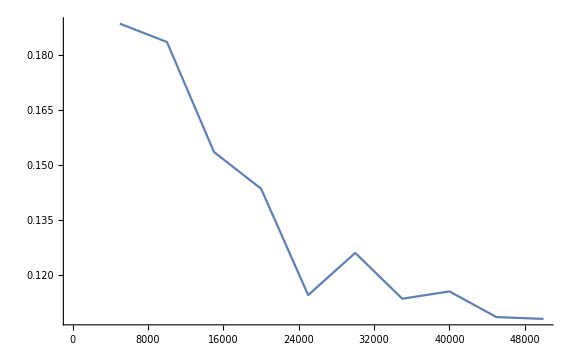
-Graphics-ErrorRateEpoch

```mathematica
Labeled[ListLinePlot[netdata["ValidationErrorRateList"],ImageSize->Large],{"ErrorRate","Epoch"},{Left,Bottom},RotateLabel->True]
```

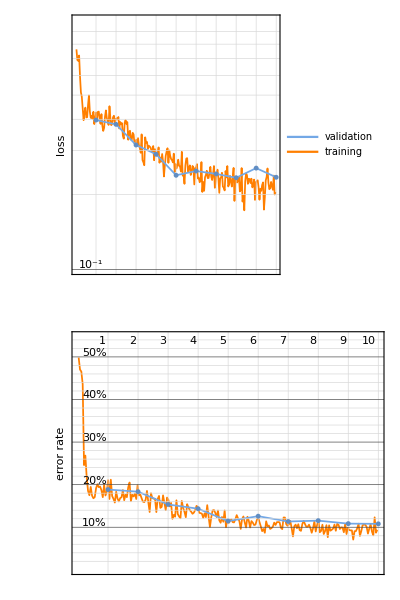
{-Graphics-,0.108}

```mathematica
netdata[{"EvolutionPlots","FinalValidationErrorRate"}]
```

```mathematica
netdata["FinalValidationErrorRate"]
```

0.108

```mathematica
net = netdata["TrainedNet"]
```

NetChain[<>]

```mathematica
NetInformation[net,"FullSummaryGraphic"]
```

-Graphics-

```mathematica
measurements=ClassifierMeasurements[net,testset1]
```

ClassifierMeasurementsObject[…]

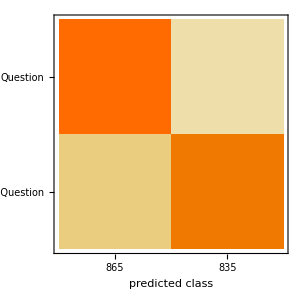

```mathematica
measurements["ConfusionMatrixPlot"]
```

Identified as questions:

```mathematica
ListAnimate[Select[measurements["MisclassifiedExamples"],Values[#]=="Not a Question"&],0.5,SaveDefinitions->True]
```

Identified as sentences:

```mathematica
ListAnimate[Select[measurements["MisclassifiedExamples"],Values[#]=="Question"&],0.5]
```

#### Microsite

```mathematica
FormPage[{{"sentence","Type a Sentence"} ->"String"}, net[#sentence]&,AppearanceRules-> {"Title" -> "Question AI"}]
```

```mathematica
CloudDeploy[

FormPage[{{"sentence","Type a Sentence"} ->"String"}, 

net[#sentence]&,

AppearanceRules-> {"Title" -> "Question AI"}],

"Questionator",
Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/zhamilya.bilyalova/Questionator]

#### Glove embedding layers

Script for running on Amazon Cloud:

Difference from my the first neural net: no NetEncoder, changing an embedding layer[97,97] to “GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data”.

```mathematica
dec=NetDecoder[{"Class",{"Question","Not a Question"}}];
emb =NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
finalNet=NetChain[{emb,DropoutLayer[0.15],GatedRecurrentLayer[512],GatedRecurrentLayer[512],DropoutLayer[0.15],GatedRecurrentLayer[512],SequenceLastLayer[],LinearLayer[32],Ramp,LinearLayer[2],SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{"Question","Not a Question"}}]];
trainednet=NetTrain[finalNet,training,All,ValidationSet->validationset, TargetDevice -> "GPU", BatchSize ->4, LearningRateMultipliers->{"1" -> 0, _ -> 1}];
```

```mathematica
glove=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"]
EmbeddingLayer[<>]
```

```mathematica
netdata2 = Import[StringJoin[NotebookDirectory[],"trainednet.wdx"]]
```

NetTrainResultsObject[<|1|>]
 |  |  |  |

```mathematica
netdata2["Properties"]
```

{BatchErrorRateList,BatchLossList,BatchSize,CheckpointingFiles,CompactErrorRateEvolutionPlot,CompactLossEvolutionPlot,ErrorRateEvolutionPlot,EvolutionPlots,FinalLearningRate,FinalRoundErrorRate,FinalRoundLoss,FinalValidationErrorRate,FinalValidationLoss,InitialLearningRate,LossEvolutionPlot,LowestValidationErrorRate,LowestValidationLoss,LowestValidationRound,MeanBatchesPerSecond,MeanInputsPerSecond,NetTrainInputForm,OptimizationMethod,RoundErrorRateList,RoundLossList,TotalBatches,TotalInputs,TotalRounds,TotalTrainingTime,TrainedNet,TrainingNet,ValidationErrorRateList,ValidationErrorRateSeries,ValidationLossList,ValidationLossSeries,VersionNumber,WeightsLearningRateMultipliers}

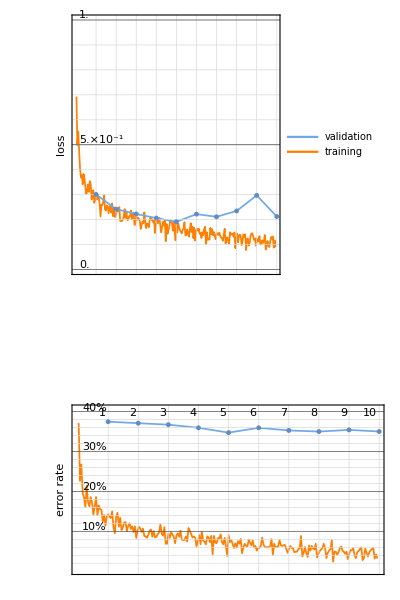
{-Graphics-,0.349933}

```mathematica
netdata2[{"EvolutionPlots","FinalValidationErrorRate"}]
```

```mathematica
net2 = netdata2["TrainedNet"]
```

NetChain[<>]

```mathematica
NetInformation[net2,"FullSummaryGraphic"]
```

-Graphics-

```mathematica
Classify[net,{"Station wagon.","What.","So your clients want something for the lobby of their new corporate headquarters.","Well what's the point of waiting.","It's sixth century B.C.  Do you like the period.","Dance.","Okay.","What are you going to do."}]
```

{Question,Question,Question,Question,Question,Question,Question,Question}

```mathematica
Classify[net,{"How is the career growth of a bank PO.","How do I concentrate better on my studies.","How do I prevent myself from eating too much sweets.","What are some good books for DBMS beginners.","What is the best way to learn math. How can I learn math more effectively.","How can I earn money through YouTube.","What is the role of ethics in corporate governance."}]
```

{Question,Question,Question,Question,Question,Question,Question}

```mathematica
Classify[net,{"I know you did it, but how?","Me","Okay","Are you going to the shop?","What that question ment"}]
```

{Question,Question,Question,Question,Question}

```mathematica
Classify[net,"I loved this lunch"]
```

Not a Question

#### ELMo net without punctuation

```mathematica
questionsWithoutQuestionsNoP = StringReplace[Normal[StringReplace[questions,{"?"->"."}]],PunctuationCharacter:>""]
normalLinesNoP=

StringReplace[Normal[Join[wikiS,RandomSample[Complement[sentences,questions][[80;;64213]],19653]]],PunctuationCharacter:>""]

Print["creating data set..."]

trainingqsNoP=Thread[#->"Question"]&/@questionsWithoutQuestionsNoP;

trainingnotqsNoP=Thread[#->"Not a Question"]&/@normalLinesNoP;

trainingJoinedNoP=Join[trainingqsNoP,trainingnotqsNoP];

trainingNoP=RandomSample[trainingJoinedNoP,20000];

validationsetNoP=RandomSample[Complement[trainingJoinedNoP,trainingNoP],2000];

testsetNoP=RandomSample[Complement[trainingJoinedNoP,validationsetNoP,trainingNoP],1700]
```

{How is the career growth of a bank PO,How do I concentrate better on my studies,How do I prevent myself from eating too much sweets,What are some good books for DBMS beginners,46299,Its sixth century BC  Do you like the period,Dance,Okay,What are you going to do}
 |  |  |  |

{Artifice Magazine was a nonprofit literary magazine based in Chicago Illinois,46305,Lemme out of this coffin}
 |  |  |  |

creating data set...

{Im a captain→Not a Question,REPEAT→Not a Question,Who is eligible for taking MCAT exams→Question,What are pseudo question and what are some examples→Question,Its okay honey→Not a Question,With all the shit she kept doing→Not a Question,What it is meant by Informatica active and passive transformation→Question,Would you say you understand Josephine→Question,I tell you stuff that I dont tell anyone else→Not a Question,It is only too possible→Not a Question,How can I teach myself Mandarin for free→Question,What are some examples of epithelial tissues→Question,Did you even to try to negotiate→Question,I can come down next week→Not a Question,Im sorry about Saturday Dad→Not a Question,ndwelling an 1893 poem by Thomas Edward Brown→Not a Question,Some asshole wrote a poem about that once→Not a Question,Will the new Rs 2000 notes carry a nano GPS chip Will it really Help→Question,Hes with a bunch of guys who want to sneak into the city tonight→Not a Question,You shouted at me in the auditorium when I read my essay→Not a Question,Why do you always disrespect me like that→Question,The most highlyregarded period of production is about 16401740→Not a Question,Havent you forgotten something→Question,Shut your mouth→Not a Question,You remembered→Not a Question,Why do Taiwanese people dislike China→Question,Why do some answers get collapsed on Quora→Question,No no Im not angry Im not Im just thrown Im→Not a Question,Maybe like work in a petting zoo or something→Not a Question,The terms Order of Saint Benedict and Benedictine Order are however also used to refer to all Benedictine communities collectively sometimes giving the incorrect impression that there exists a generalate or motherhouse with jurisdiction over them→Not a Question,What baby→Question,Carbon dioxide→Question,How do converting waste lubricant oil to diesel fuel→Question,Dont give me this we were partners→Not a Question,How can I learn how to be happy→Question,Indian School of Business YLP I have a year to go before I apply for YLP can somebody give me tips to boost my resume→Question,Over and over→Not a Question,Is he not tired→Question,Shall we→Question,Rose you work too hard→Not a Question,Show her in→Not a Question,Do you think that Donald Trump would be the worst president the United States would ever have→Question,They are commonly known for their extensive tunneling activities→Not a Question,Why are diamonds valuable→Question,Whatre you laughing about→Question,Who didnt→Question,In linguistics periphrasis  is the usage of multiple separate words to carry the meaning of prefixes suffixes or verbs among other things where either would be possible→Not a Question,Forget her youre mine→Not a Question,Excuse me Skipper What about time→Question,Know what→Question,Vertical devices are known as tanning booths or standup sunbeds→Not a Question,The activities on a pig farm depend on the husbandry style of the farmer and range from very little intervention as when pigs are allowed to roam villages or towns and dispose of garbage to intensive systems where the pigs are contained in a building for the majority of their lives→Not a Question,If a bra is worn with a halter top it is generally either strapless or of halterneck construction itself so as to avoid exposing the back straps of a typical bra→Not a Question,The terms pinnation and pennation are cognate and although they are sometimes used distinctly there is no consistent difference in the meaning or usage of the two words→Not a Question,Nice mouth you got there Mom but I  Im not goin through this again→Not a Question,Tonight→Question,What is the best way to monetize user generated video content→Question,How do I develop my presence of mind→Question,Am I supposed to worry about whats in the refrigerator too→Question,The start and end points of time for a night vary based on factors such as season latitude longitude and time zone→Not a Question,Finished lumber is supplied in standard sizes mostly for the construction industry  primarily softwood from coniferous species including pine fir and spruce collectively sprucepinefir cedar and hemlock but also some hardwood for highgrade flooring→Not a Question,Do CBSE students suffer in class 12 they get 90 in class 10 and 50 in boards→Question,Dirt is unclean matter especially when in contact with a persons clothes skin or possessions when they are said to become dirty→Not a Question,Will an iPhone 7 plus bought through Tmobile work in India→Question,maybe she had an accident→Not a Question,What are the common mistakes that new sellers on eBay make→Question,The bone is formed from a fusion of left and right processes and the point where these sides join the mandibular symphysis is still visible as a faint ridge in the midline→Not a Question,If I delete my whisper account can the other person still see my messages→Question,Shell forget about us eventually→Not a Question,The third stage of labor can be managed actively with several standard procedures or it can be managed expectantly also known as physiological management or passive management the latter allowing the placenta to be expelled without medical assistance→Not a Question,A girls gotta know how to defend herself dont she→Question,Opportunity may refer to
Opportunity rover a robotic rover active on the planet Mars since 2004
The Opportunity a 17thcentury play
Opportunity→Not a Question,Theorists who adopt this interpretation think of probability as a physical propensity or disposition or tendency of a given type of physical situation to yield an outcome of a certain kind or to yield a long run relative frequency of such an outcome→Not a Question,Did I have anything to say about it→Question,Do you understand that→Question,Why is sex education considered a taboo topic in India→Question,What are some major social faux pas to avoid when visiting Bangladesh→Question,Larry from the States→Not a Question,Wheres Clark→Question,Why is it that we havent been able to tap into the full potential of our brains→Question,I had to dive in and save him→Not a Question,Groovy→Not a Question,A suit was gone→Not a Question,What did you feel Brian when you first got there→Question,Doesnt make much sense does it→Question,What are new research topics in geotechnical engineering for master degree→Question,A metaphor is a figure of speech that directly refers to one thing by mentioning another for rhetorical effect→Not a Question,Originally meaning strange or peculiar queer came to be used pejoratively against those with samesex desires or relationships in the late 19th century→Not a Question,Do I make you nervous→Question,Emotion is also linked to behavioral tendency→Not a Question,He promoted reconciliation between the countrys indigenous tribal groups and its European minority although his relations with the Kenyan Indians were strained→Not a Question,Look Brian a photographer→Not a Question,Tell Mother beware→Not a Question,This ship its crazy trying to go fastern light thats like the Tower of Babel→Not a Question,Jean may refer to→Not a Question,Youre a free thinker→Not a Question,Overthrow structure the crowning section of ornamental wrought iron work which forms a decorative crest above a wrought iron gate→Not a Question,25 less than 300 is what  more than 200→Question,How can I hack WiFi using a command prompt→Question,Thats not it→Not a Question,Whats the difference between Italian Fascism and Nazism→Question,How do you download Pokémon GO→Question,Woodhull may refer to→Not a Question,How do I apply for a summer internship→Question,Do girls really like tall guys→Question,One of them is used as the pedestal of the Bronze Horseman in Saint Petersburg Russia→Not a Question,Shadowbox is a DVD and accompanying EP by The Crxshadows→Not a Question,Can banks run a 247 operation→Question,Is it so wrong to go up to a guy and tell him that he is beautiful→Question,I cant→Not a Question,now what→Question,Will I grow taller at 15→Question,For example in India licensed moneylenders are governed by Money Lenders Acts of respective states→Not a Question,A plant is often termed a weed when it has one or more of the following characteristics→Not a Question,What mythical creatures are in the Bible→Question,What is it like flying first class→Question,Whats your favourite anime→Question,What are the safety precautions on handling shotguns proposed by the NRA in North Carolina→Question,Who will win in Liverpool VS AC Milan International Champions Cup→Question,Sometimes prequels play on the audiences knowledge of what will happen next using deliberate references to create dramatic irony→Not a Question,Why dont you just do it out of the kindness of your heart→Question,But for you→Question,Sometimes which→Question,Tell me in sadness who is that you love→Not a Question,It is objectoriented classbased and reflective→Not a Question,Most lemonade varieties can be separated into two distinct types cloudy or clear each is known simply as lemonade or a cognate in countries where dominant→Not a Question,Listen what Im about to tell you Im telling you in confidence okay→Question,Its not finished→Not a Question,How are design decisions made at Google→Question,Im back here arent I→Question,What is another word for I→Question,How can I dual boot Windows 7 and Linux→Question,A disassembler is a computer program that translates machine language into assembly languagethe inverse operation to that of an assembler→Not a Question,Do two photons emitted from two atoms 1 meter apart have a higher probability of being found further apart after one second Is this an arrow of time→Question,What TV series were cancelled too soon→Question,Why on earth do you say that→Question,You think you can stitch me up on you own→Question,I forgot my ATM PIN What do I do→Question,Are you really going to drink that stuff→Question,thats when you start praying all the time→Not a Question,Purple drank a recreational drug→Not a Question,Are you afraid→Question,What is magnetic moment of an electron→Question,Panties were originally designed to cover the entire lower half of the female torso since the 1970s panties have had either no legs or in some cases very short ones and have become increasingly brief over time→Not a Question,That light is not daylight I know it I→Not a Question,Polemics are mostly seen in arguments about controversial topics→Not a Question,The last time I heard from her she was living in San Francisco→Not a Question,Kid over there caught the case→Not a Question,How do I get rid of excessive weight→Question,But come on Harry whats the real reason→Question,Maiman at Hughes Research Laboratories based on theoretical work by Charles Hard Townes and Arthur Leonard Schawlow→Not a Question,How long would it actually take to travel to Mars→Question,At least no ones gonna see how bad you are→Not a Question,Dont let us make you nervous or nothinwe know you gotta job to do→Not a Question,SPOILERS What happened at the end of Wolf of Wall Street→Question,When is the best time to visit France→Question,Roofing work can be physically demanding because it involves heavy lifting as well as climbing bending and kneeling frequently in very hot weather→Not a Question,What was it→Question,What positions I am eligible to apply at Oracle→Question,A millwright is a high precision craftsman or tradesman who installs dismantles repairs reassembles and moves machinery in factories power plants and construction sites→Not a Question,Then why did you quit→Question,Historically a liquiddriven escapement was used for a washstand design in ancient Greece and the Hellenistic world particularly Ptolemaic Egypt while the medieval Chinese beginning in the Tang dynasty and culminating during the Song dynasty applied liquiddriven escapements to clockworks→Not a Question,Now how are you going to do that→Question,Just some rich Anglo out on the lake→Not a Question,Spreading from Italian to the other European languages the term was long used largely interchangeably with arabesque and moresque for types of decorative patterns using curving foliage elements→Not a Question,Our revels now are ended You disappoint me Emma→Not a Question,Theyre no friends of mine→Not a Question,How do I know if Im good→Question,What do you want me for anyway→Question,A consultant is usually an expert or an experienced professional in a specific field and has a wide knowledge of the subject matter→Not a Question,Is it safe to smoke weed once a week→Question,He also agreed to waive his performance fee for full ownership of the Sesame Street Muppets and to split any revenue they generated with the Childrens Television Workshop renamed to the Sesame Workshop in 2000 the series nonprofit producer→Not a Question,Dont tell me youre waiting for lightning to strike→Not a Question,Why are you driving→Question,Whose fault is the illegal construction developer or administration→Question,Mister OHiggins I wonder if I know your good father→Question,Thank you for calling the white House→Not a Question,Mrs Christian→Not a Question,Because of these persistent natural forces sea walls need to be maintained and eventually replaced to maintain their effectiveness→Not a Question,What government will do from old currency→Question,What is it like to be a lesbian in India→Question,You get it quick→Not a Question,Welsh may refer to→Not a Question,This militant irony or sarcasm often professes to approve of or at least accept as natural the very things the satirist wishes to attack→Not a Question,The inference rules are commonly specified by means of an ontology language and often a description logic language→Not a Question,Youd make a pisspoor lawyer→Not a Question,My ITRV has place as pune instead of bangalore can I strike it off and post it→Question,What was I wearing→Question,In firearms rifling is the helical groove pattern that is machined into the internal bore surface of a guns barrel for the purpose of exerting torque and thus imparting a spin to a projectile around its longitudinal axis during shooting→Not a Question,What is the best working model that easily can make by 8 class student→Question,Germany classifies Scientology groups as an anticonstitutional sect→Not a Question,retending Eric Clapton song a 1989 rock song written and composed by Jerry Lynn Williams
→Not a Question,How do you make a site like Facebook→Question,How did you end up here→Question,You sure dont fit in down on the Boulevard lookin like you do→Not a Question,I want to improve my English→Question,Other treatment options may target airway inflammation or may promote mucus expectoration→Not a Question,What subscription payment option should i use for my mobile app for non US markets→Question,WHY→Question,It is found in temperate and tropical waters across the globe in the epipelagic and mesopelagic zones→Not a Question,If that object withstands ablation from its passage through the atmosphere as a meteor and impacts with the ground it is then called a meteorite→Not a Question,Sepsis is more common among males than females→Not a Question,Next time you try that Mr Mitchell  dont→Not a Question,Is it possible for a girl to like you but be a really slow texter→Question,Written Chinese the writing system used for Chinese

Chinese cuisine styles of food originating from China
American Chinese cuisine→Not a Question,What are some ways to hack a Facebook account→Question,How do I see if someone visited my Facebook profile→Question,Whats he going to say→Question,How much kale is in a bunch→Question,What UK online shopping stores dont require a CVV code→Question,Vales or Vale is a surname→Not a Question,Where can I get branded surplus garments in Bangalore→Question,So does he→Not a Question,Lets just kick it here alright→Question,If he talks or writes a note BOOTH EARL BOOTH EARL BOOTH EARL EARL BOOTH EARL BOOTH EARL BOOTH BOOTH EARL BOOTH EARL BOOTH EARL BOOTH EARL BOOTH BOOTH m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 m495 u7327 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7327 u7331 u7327 u7331 u7327 u7331 u7331 u7327 u7327 u7334 u7327 u7334 u7327 u7334 u7327 u7334 u7327 u7334 u7332 u7327 u7332 u7327 u7332 u7327 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7332 u7327 u7327 u7332 u7327 u7327 u7332 u7327 u7332 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7330 u7327 u7330 u7327 u7330 u7327 u7327 u7330 u7327 u7330 u7327 u7330 u7327 u7330 u7330 u7327 u7327 u7333 u7327 u7333 u7327 u7327 u7333 u7327 u7333 u7327 u7333 u7327 u7333 u7333 u7327 u7333 u7333 u7327 u7333 u7327 u7333 u7327 u7327 u7327 u7333 u7327 u7327 u7333 u7327 u7333 u7327 u7333 u7327 u7333 u7327 u7330 u7328 u7328 u7330 u7330 u7328 u7328 u7330 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7330 u7328 u7330 u7330 u7328 u7330 u7328 u7330 u7328 u7330 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7328 u7329 u7329 u7328 u7331 u7334 u7331 u7334 u7331 u7331 u7334 u7331 u7334 u7334 L475646 L475645 L475644 L475643 L475641 L475640 L475639 L475638 L475637 L475636 L475635 L475634 L475633 L475632 L475631 L478251 L478250 L478249 L478248 L478247 L478246 L478245 L478244 L478243 L478242 L478723 L478722 L478701 L478700 L478699 L478698 L478686 L478685 L478684 L478683 L478682 L478681 L478680 L478280 L478279 L478278 L478277 L478276 L478275 L478274 L478540 L478539 L478533 L478532 L478531 L478530 L478529 L478528 L478527 L478526 L478525 L478515 L478514 L478513 L478512 L478511 L478510 L478509 L478508 L478491 L478490 L478489 L478484 L478483 L478482 L478481 L478478 L478477 L478476 L478475 L478474 L478469 L478468 L478467 L478466 L478297 L478296 L478295 L478294 L478293 L478292 L478291 L478290 L478289 L478288 L478287 L478286 L478285 L478284 L478283 L478783 L478782 L478778 L478777 L478321 L478320 L478209 L478208 L478207 L478206 L478205 L478201 L478200 L478199 L478198 L478184 L478183 L478182 L478181 L478180 L478179 L478178 L478177 L478176 L478175 L478662 L478661 L478660 L478659 L478658 L478657 L478301 L478300 L478820 L478819 L478818 L478817 L478816 L478815 L478814 L478813 L478812 L478811 L478810 L478809 L478808 L478807 L478806 L478804 L478803 L478801 L478800 L478799 L478798 L478797 L478796 L478795 L478791 L478790 L478781 L478780 L478751 L478750 L478749 L478747 L478746 L478745 L478744 L478743 L478742 L478741 L478736 L478735 L478677 L478676 L478675 L478674 L478673 L478672 L478671 L478670 L478669 L478668 L478643 L478642 L478636 L478635 L478634 L478629 L478628 L478623 L478622 L478621 L478620 L478619 L478618 L478617 L478616 L478614 L478613 L478612 L478611 L478610 L478609 L478607 L478606 L478605 L478604 L478603 L478602 L478601 L478600 L478599 L478598 L478595 L478594 L478593 L478592 L478591 L478590 L478589 L478588 L478587 L478586 L478585 L478584 L478583 L478582 L478581 L478580 L478579 L478578 L478577 L478576 L478575 L478574 L478573 L478572 L478571 L478570 L478569 L478568 L478567 L478566 L478565 L478564 L478563 L478562 L478561 L478560 L478559 L478558 L478557 L478556 L478555 L478554 L478553 L478552 L478551 L478550 L478503 L478502 L478501 L478500 L478499 L478498 L478497 L478471 L478470 L478465 L478464 L478462 L478461 L478460 L478459 L478452 L478451 L478450 L478444 L478443 L478442 L478441 L478440 L478439 L478438 L478435 L478434 L478433 L478432 L478431 L478430 L478429 L478428 L478427 L478426 L478425 L478424 L478423 L478422 L478421 L478420 L478419 L478418 L478417 L478416 L478412 L478411 L478410 L478409 L478408 L478407 L478406 L478405 L478404 L478403 L478402 L478401 L478400 L478399 L478398 L478397 L478396 L478395 L478394 L478393 L478392 L478391 L478390 L478389 L478388 L478387 L478386 L478385 L478384 L478383 L478382 L478381 L478380 L478379 L478378 L478377 L478376 L478375 L478374 L478373 L478372 L478371 L478370 L478369 L478368 L478367 L478366 L478365 L478364 L478363 L478362 L478360 L478359 L478358 L478357 L478356 L478355 L478354 L478353 L478352 L478351 L478350 L478327 L478326 L478325 L478324 L478323 L478314 L478313 L478312 L478311 L478310 L478309 L478308 L478307 L478233 L478232 L478231 L478230 L478229 L478228 L478227 L478226 L478225 L478224 L478223 L478222 L478213 L478212 L478196 L478195 L478194 L478193 L478192 L478191 L478188 L478187 L478186 L478185 L478174 L478173 L478172 L478170 L478169 L478168 L478167 L478143 L478142 L478140 L478139 L478138 L478137 L478135 L478134 L478124 L478123 L478122 L478120 L478119 L478118 L478117 L478116 L478115 L478114 L478113 L478112 L478111 L478110 L478109 L478105 L478104 L478103 L478102 L478101 L478100 L478099 L478098 L478097 L478096 L478095 L478094 L478088 L478087 L478086 L478085 L478084 L478083 L478082 L478081 L478080 L478079 L478078 L478343 L478342 L478341 L478340 L478339 L478338 L478758 L478757 L478756 L478755 L478667 L478666 L478665 L478664 L478663 L478656 L478655 L478654 L478653 L478652 L478651 L478650 L478649 L478648 L478647 L478645 L478644 L478488 L478487 L478486 L478480 L478479 L478473 L478472 L478535 L478534 L478523 L478522 L478521 L478520 L478519 L478518 L478346 L478345 L478271 L478270 L478269 L478268 L478262 L478261 L478235 L478234 L478092 L478091 L478090 L478089 L478775 L478774 L478773 L478772 L478771 L478334 L478333 L478332 L478331 L478330 L478329 L478328 L478204 L478203 L478164 L478163 L478162 L478161 L478160 L478158 L478157 L478156 L478155 L478154 L478149 L478148 L478221 L478220 L478219 L478218 L478217 L478216 L478215 L478214 L477745 L477744 L477743 L477742 L477741 L477740 L477739 L477737 L477736 L477735 L477734 L477733 L477732 L477731 L477381 L477380 L477459 L477458 L477457 L477456 L477455 L477454 L477453 L477452 L477451 L477450 L477449 L477448 L478057 L478056 L478055 L478054 L477688 L477687 L477686 L477474 L477473 L478074 L478073 L478072 L478071 L478070 L478026 L478025 L478023 L478022 L478019 L478018 L478017 L477973 L477972 L477959 L477958 L477929 L477928 L477927 L477925 L477924 L477881 L477880 L477873 L477872 L477869 L477868 L477867 L477865 L477864 L477863 L477862 L477861 L477860 L477859 L477858 L477857 L477856 L477855 L477854 L477853 L477847 L477846 L477845 L477844 L477843 L477842 L477841 L477840 L477839 L477838 L477837 L477834 L477833 L477831 L477830 L477829 L477828 L477827 L477826 L477825 L477802 L477801 L477800 L477799 L477798 L477784 L477783 L477782 L477781 L477780 L477779 L477778 L477773 L477772 L477771 L477770 L477769 L477768 L477767 L477766 L477716 L477715 L477714 L477710 L477709 L477708 L477707 L477706 L477705 L477704 L477703 L477702 L477701 L477700 L477669 L477668 L477667 L477666 L477664 L477663 L477662 L477661 L477660 L477590 L477589 L477586 L477585 L477584 L477583 L477582 L477581 L477580 L477579 L477574 L477573 L477570 L477569 L477568 L477567 L477566 L477565 L477564 L477563 L477562 L477561 L477560 L477548 L477547 L477546 L477528 L477527 L477524 L477523 L477522 L477517 L477516 L478068 L478067 L478066 L478065 L478064 L478063 L478062 L478021 L478020 L478005 L478004 L478003 L478002 L477996 L477995 L477994 L477971 L477970 L477969 L477968 L477967 L477966 L477965 L477964 L477676 L477675 L477504 L477503 L477502 L477501 L477500 L477499 L477498 L477497 L477469 L477468 L477467 L477466 L477465 L477464 L477463 L477462 L477447 L477446 L477439 L477438 L477437 L477417 L477416 L477396 L477395 L477940 L477939 L477938 L477937 L477756 L477755 L477754 L477753 L477752 L477751 L477726 L477725 L477724 L477723 L477640 L477639 L477637 L477636 L477494 L477493 L477492 L477491 L477490 L477489 L477488 L477487 L477486 L477485 L477484 L477481 L477480 L477479 L477478 L477477 L477819 L477818 L477815 L477814 L477813 L477812 L477811 L477810 L477809 L477412 L477411 L477402 L477401 L477398 L477397 L477391 L477390 L477389 L477388 L477387 L477385 L477384 L477383 L477382 L477993 L477992 L477991 L477953 L477952 L477951 L477647 L477646 L477645 L477644 L477643 L477642 L477641 L477891 L477890 L477889 L477888 L477536 L477535 L477534 L477533 L477532 L477823 L477822 L477821 L477820 L477634 L477633 L477433 L477432 L477431 L477430 L477429 L477428 L477427 L477378 L477377 L477375 L477374 L477373 L477372 L477371 L480093 L480092 L479933 L479932 L479729 L479728 L479727 L479726 L479725 L479724 L479723 L479719 L479718 L479716 L479715 L480192 L480191 L480190 L480189 L480187 L480186 L480126 L480125 L480116 L480115 L479722 L479721 L479675 L479674 L479762 L479761 L479760 L479759 L479758 L479756 L479755 L479753 L479752 L479751 L479750 L479749 L479748 L479747 L479743 L479742 L479741 L479740 L480171 L480170 L480168 L480167 L480166 L480163 L480162 L479579 L479578 L480165 L480164 L480150 L480149 L480112 L480111 L480110 L480109 L480108 L480107 L480096 L480095 L480226 L480225 L480030 L480029 L480028 L480027 L480024 L480023 L479554 L479553 L479552 L479551 L479549 L479548 L479545 L479544 L479543 L479542 L479541 L479540 L479539 L479536 L479535 L479534 L480224 L480223 L480222 L480020 L480019 L480018 L480017 L480196 L480195 L480194 L480184 L480183 L480182 L480181 L480022 L480021 L479993 L479992 L479991 L479990 L479989 L479988 L479987 L479986 L479985 L479984 L479575 L479574 L479572 L479571 L479570 L479569 L479568 L479567 L479566 L479565 L479564 L479563 L479562 L479561 L479560 L479559 L479547 L479546 L479538 L479537 L480013 L480012 L480011 L480010 L480009 L480008 L480007 L480006 L480004 L480003 L480002 L480001 L480000 L479999 L479998 L479997 L479996 L479995 L479994 L480179 L480178 L479937 L479936 L479612 L479611 L479610 L479608 L479607 L479606 L479605 L479604 L479807 L479806 L479804 L479803 L479802 L479801 L479626 L479625 L479596 L479595 L479594 L479590 L479589 L479588 L479587 L479586 L479585 L479584 L479583 L480199 L480198 L480197 L479710 L479709 L479699 L479698 L479697 L479696 L479666 L479665 L479661 L479660 L479657 L479656 L479655 L479649 L479648 L480288 L480287 L480286 L480285 L480284 L480283 L480277 L480276 L480275 L480270 L480269 L480268 L480267 L480266 L480265 L480264 L480263 L480261 L480260 L480145 L480144 L480143 L480142 L480141 L480140 L480139 L480138 L480137 L480135 L480134 L480133 L480132 L480131 L480124 L480123 L480122 L480120 L480119 L480100 L480099 L480098 L480089 L480088 L480087 L480086 L480085 L480084 L480083 L480082 L480081 L480080 L480079 L480078 L480077 L480076 L480075 L480074 L480073 L480072 L480071 L480070 L480069 L480068 L480067 L480057 L480056 L480055 L480054 L480053 L480044 L480043 L479979 L479978 L479973 L479972 L479971 L479970 L479969 L479968 L479967 L479962 L479961 L479952 L479951 L479950 L479949 L479948 L479947 L479940 L479939 L479935 L479934 L479930 L479929 L479928 L479923 L479922 L479921 L479898 L479897 L479893 L479892 L479891 L479890 L479889 L479888 L479887 L479886 L479884 L479883 L479882 L479881 L479879 L479878 L479877 L479876 L479874 L479873 L479872 L479871 L479870 L479869 L479868 L479865 L479864 L479862 L479861 L479860 L479859 L479858 L479857 L479856 L479855 L479854 L479852 L479851 L479850 L479849 L479847 L479846 L479811 L479810 L479809 L479808 L479783 L479782 L479771 L479770 L479701 L479700 L479684 L479683 L479682 L479680 L479679 L479678 L479677 L479672 L479671 L479642 L479641 L479640 L479639 L479638 L479636 L479635 L479620 L479619 L479618 L479617 L479614 L479613 L479601 L479600 L479599 L480238 L480237 L480236 L480235 L480234 L480233 L480232 L480231 L480230 L480210 L480209 L480161 L480160 L480159 L480158 L480153 L480152 L480106 L480105 L480104 L480103 L480102 L480038 L480037 L480036 L480035 L480034 L479844 L479843 L479842 L479841 L479840 L479839 L479838 L479837 L479836 L479835 L479834 L479833 L479832 L479831 L479830 L479828 L479827 L479825 L479824 L479823 L479795 L479794 L479793 L479792 L479791 L479790 L479789 L479788 L479787 L479786 L479603 L479602 L479598 L479597 L479582 L479581 L479580 L479523 L479522 L480255 L480254 L480253 L480252 L480251 L480250 L480207 L480206 L479958 L479957 L479956 L479955 L479670 L479669 L479516 L479515 L479514 L479513 L479512 L479511 L479510 L479509 L479508 L480305 L480304 L480303 L480302 L480299 L480298 L480297 L480296 L480295 L480294 L480293 L480853 L480852 L480851 L480850 L480849 L480848 L480847 L480846 L480845 L480844 L480843 L480842 L481180 L481179 L481178 L481177 L481176 L481175 L481174 L481173 L481172 L481171 L481170 L481169 L481168 L481167 L481166 L481148 L481147 L481088 L481087 L481086 L481082 L481081 L481080 L481079 L481075 L481074 L481073 L481072 L481071 L481070 L481069 L480937 L480936 L480935 L480934 L480933 L480913 L480912 L480911 L480903 L480902 L480886 L480885 L480642 L480641 L480640 L480639 L480638 L480637 L480636 L480635 L480634 L480633 L480632 L480631 L480426 L480425 L480424 L480423 L480422 L480421 L480420 L480419 L480418 L480417 L480383 L480382 L480364 L480363 L480360 L480359 L480347 L480346 L480345 L480344 L480343 L480342 L480341 L480340 L480339 L480338 L481052 L481051 L481050 L481049 L481048 L481047 L481015 L481014 L481013 L481012 L481010 L481009 L481008 L481007 L481006 L481005 L481004 L481003 L481002 L481001 L481000 L480996 L480995 L480994 L480993 L480992 L480991 L480984 L480983 L480982 L480981 L480980 L480979 L480978 L480977 L480976 L480975 L480974 L480973 L480921 L480920 L480919 L480884 L480883 L480882 L480881 L480764 L480763 L480762 L480761 L480760 L480759 L480758 L480757 L480756 L480755 L480754 L480753 L480752 L480751 L480750 L480749 L480748 L480747 L480746 L480745 L480744 L480743 L480742 L480741 L480740 L480739 L480738 L480737 L480736 L480735 L480734 L480733 L480588 L480587 L480586 L480585 L480584 L480583 L480582 L480581 L480580 L480579 L480571 L480570 L480565 L480564 L480563 L480798 L480797 L480796 L480795 L480794 L480793 L480792 L480791 L480790 L480789 L480788 L480787 L480320 L480319 L480318 L480317 L480316 L480315 L480314 L480313 L481212 L481211 L481210 L481209 L481206 L481205 L480898 L480897 L480888 L480887 L480477 L480476 L480453 L480452 L480700 L480699 L480698 L480697 L480696 L480695 L480694 L480693 L480692 L480691 L480690 L480689 L480416 L480415 L480414 L480413 L480412 L480411 L480410 L480409 L480408 L480407 L480406 L480405 L480404 L480403 L480402 L480401 L480400 L480399 L480398 L480397 L480396 L480395 L480394 L480393 L480392 L480391 L480390 L480389 L480388 L480358 L480357 L480349 L480348 L481204 L481203 L481202 L481046 L481045 L481044 L480989 L480988 L480524 L480523 L480522 L480487 L480486 L480609 L480608 L480599 L480598 L480597 L480596 L480595 L480592 L480591 L480521 L480520 L480519 L480518 L480517 L480516 L480515 L480514 L480499 L480498 L480485 L480484 L480483 L480482 L480481 L480480 L480479 L480478 L480475 L480474 L480471 L480470 L480469 L480468 L480467 L480466 L480465 L480490 L480489 L480460 L480459 L480458 L480457 L480456 L480455 L480454 L480451 L480450 L480449 L480448 L480445 L480444 L480443 L480442 L480440 L480439 L480438 L480437 L480436 L480435 L480434 L480433 L481040 L481039 L481038 L481037 L481036 L481035 L481032 L481031 L480717 L480716 L480715 L480714 L480713 L480712 L480711 L480710 L480709 L480708 L480707 L480706 L480705 L480704 L480703 L480702 L480701 L480601 L480600 L481067 L481066 L481065 L481064 L481063 L481060 L481059 L481058 L481057 L481056 L481055 L481054 L481053 L480918 L480917 L480916 L480915 L480914 L480728 L480727 L481189 L481188 L481187 L481186 L481165 L481164 L481163 L481162 L481161 L481160 L481159 L481158 L481157 L481156 L481111 L481110 L481109 L481108 L481107 L481106 L481105 L481104 L481103 L481102 L481101 L481100 L481099 L481098 L481096 L481095 L481094 L481093 L481092 L481091 L481090 L480963 L480962 L480959 L480958 L480957 L480956 L480955 L480953 L480952 L480951 L480931 L480930 L480929 L480928 L480927 L480926 L480925 L480924 L480910 L480909 L480908 L480907 L480906 L480905 L480904 L480880 L480879 L480878 L480877 L480876 L480875 L480874 L480858 L480857 L480856 L480855 L480827 L480826 L480825 L480823 L480822 L480821 L480820 L480819 L480818 L480817 L480816 L480815 L480814 L480813 L480812 L480811 L480810 L480809 L480805 L480804 L480779 L480778 L480777 L480776 L480775 L480774 L480773 L480772 L480771 L480770 L480769 L480768 L480767 L480766 L480726 L480725 L480724 L480723 L480722 L480676 L480675 L480674 L480673 L480672 L480671 L480670 L480669 L480668 L480667 L480666 L480665 L480664 L480663 L480662 L480661 L480660 L480659 L480658 L480657 L480656 L480655 L480654 L480653 L480652 L480651 L480650 L480649 L480626 L480625 L480624 L480621 L480620 L480619 L480618 L480617 L480616 L480615 L480614 L480613 L480612 L480611 L480606 L480605 L480604 L480603 L480602 L480554 L480553 L480552 L480551 L480550 L480549 L480548 L480538 L480537 L480536 L480534 L480533 L480532 L480493 L480492 L480463 L480462 L480461 L480943 L480942 L480941 L480873 L480872 L480871 L480870 L480869 L480868 L480867 L480860 L480859 L480547 L480546 L480545 L480543 L480542 L480541 L480540 L481043 L481042 L481041 L481029 L481028 L481027 L481023 L481022 L481021 L481020 L481017 L481016 L480986 L480985 L480324 L480323 L480322 L480301 L480300 L480950 L480949 L480948 L480947 L480946 L480945 L480944 L480896 L480895 L480894 L480864 L480863 L480862 L480839 L480838 L480837 L480836 L480835 L480834 L480833 L480832 L480831 L480830 L480829 L480828 L481462 L481461 L481460 L481459 L481448 L481447 L481446 L481445 L481444 L481443 L481362 L481361 L481360 L481871 L481870 L481698 L481697 L481696 L481695 L481694 L481657 L481656 L481655 L481431 L481430 L481429 L481749 L481748 L481747 L481746 L481745 L481744 L481743 L481742 L481741 L481740 L481739 L481591 L481590 L481437 L481436 L481435 L481297 L481296 L481365 L481364 L481363 L481259 L481258 L481257 L481256 L481251 L481250 L481249 L481248 L481247 L481246 L481319 L481318 L481317 L481316 L481261 L481260 L481236 L481235 L481234 L481233 L481843 L481842 L481772 L481771 L481716 L481715 L481351 L481350 L481343 L481342 L481861 L481860 L481859 L481839 L481838 L481837 L481836 L481835 L481834 L481833 L481832 L481831 L481830 L481829 L481828 L481827 L481825 L481824 L481823 L481822 L481821 L481820 L481819 L481818 L481817 L481816 L481815 L481814 L481813 L481812 L481811 L481810 L481808 L481807 L481806 L481805 L481804 L481803 L481802 L481801 L481776 L481775 L481774 L481773 L481770 L481769 L481768 L481767 L481764 L481763 L481762 L481761 L481685 L481684 L481683 L481682 L481681 L481680 L481679 L481678 L481677 L481676 L481649 L481648 L481647 L481646 L481645 L481644 L481643 L481642 L481641 L481640 L481639 L481580 L481579 L481578 L481577 L481576 L481570 L481569 L481568 L481567 L481566 L481565 L481564 L481563 L481562 L481561 L481560 L481508 L481507 L481466 L481465 L481327 L481326 L481325 L481324 L481323 L481322 L481321 L481292 L481291 L481290 L481289 L481288 L481287 L481286 L481285 L481284 L481283 L481282 L481281 L481280 L481279 L481278 L481277 L481275 L481274 L481273 L481272 L481271 L481270 L481269 L481267 L481266 L481265 L481264 L481553 L481552 L481551 L481550 L481400 L481399 L481398 L481537 L481536 L481535 L481534 L481523 L481522 L481305 L481304 L481303 L481302 L481301 L481457 L481456 L481455 L481454 L481453 L481452 L481451 L481450 L481449 L481758 L481757 L481756 L481755 L481754 L481753 L481752 L481751 L481675 L481674 L481673 L481672 L481470 L481469 L481312 L481311 L481310 L481309 L481485 L481484 L481483 L481482 L481481 L481480 L481479 L481478 jam →Not a Question,Do consumer product tech companies value UX research→Question,I guess hes still on the road→Not a Question,Best seat in the house  Hey Mick this is too much→Not a Question,What do Flipkarts delivery boys look for when I exchange my old lcd for a new one→Question,Am I going mad or did the word think escape your lips→Question,Then we will begin with replacing the Tibetan flag with the flag of the Motherland→Not a Question,They dont care anything for John theyre just trying to impress their friends→Not a Question,He also gave a number of novel scientific accounts of natural phenomena→Not a Question,Mung bean sprout is made from the greenishcapped mung beans
Soybean sprout is made from yellow largergrained soybean
It typically takes one week for them to become fully grown→Not a Question,Do you think hell call this week→Question,Youre playing a piano Miss Starling→Question,Evaporation is an essential part of the water cycle→Not a Question,So its an honor→Question,How do I find love→Question,I dont think hes going to be doing any bargaining with us the stupid sonofabitch→Not a Question,What are the chances to crack the civil services exam for an average student→Question,Afforestation is the establishment of a forest or stand of trees forestation in an area where there was no previous tree cover→Not a Question,This cut has its greatest popularity in Britain→Not a Question,Oh Frederick Am I a good man or am I a bad man→Question,Hazelnuts are rich in protein monounsaturated fat vitamin E manganese and numerous other essential nutrients nutrition table below→Not a Question,I think you found it quite pleasurable→Not a Question,I started riding at night to fill up my mind so that when I did sleep Id dream only of the ride and the adventure→Not a Question,The term derives from the Latin word pinna meaning feather wing or fin→Not a Question,Melancholy was one of the four temperaments matching the four humours→Not a Question,Its been eight months→Not a Question,All my life I been puttin out your fires with you givin out your snatch to every waggin dick in this town→Not a Question,Although incorporating Italian and French stylistic elements into his compositions Purcells legacy was a uniquely English form of Baroque music→Not a Question,As it passes through the point where the tangent line and the curve meet called the point of tangency the tangent line is going in the same direction as the curve and is thus the best straightline approximation to the curve at that point→Not a Question,In children deficiency causes growth retardation delayed sexual maturation infection susceptibility and diarrhea→Not a Question,Halterneck is a style of womens clothing strap that runs from the front of the garment around the back of the neck and leaves most of the back uncovered→Not a Question,How do I get into IIM A→Question,We are organized Monsieur underground like everywhere else→Not a Question,Are Sennheiser HD 201 headphones worth the £1799 I paid for them→Question,Obviation may refer to→Not a Question,Tuberculin is made out of an extract of Mycobacterium tuberculosis→Not a Question,What of our marriage→Question,A simple example is the tossing of a fair unbiased coin→Not a Question,The term originally denoted a woman whose occupation was to spin→Not a Question,The medications acamprosate disulfiram or naltrexone may also be used to help prevent further drinking→Not a Question,0th or zeroth is an ordinal for the number zero sometimes used under zerobased numbering and may refer to
0th grade another name for kindergarten
0th dimension
0th element of an array data structure in computer science
0th United States Congress also called the Congress of the Confederation
January 0 or January 0th an alternate name for December 31
Zeroth law of thermodynamics
Zerothorder logic
Zeroth law of robotics an addition to Isaac Asimovs Three Laws of Robotics
Zeroth order approximation
Zeroth the fastest demo or highest score on a level or episode in N video game→Not a Question,What is the proper way to format a header in MLA style→Question,he term Talmud normally refers to the collection of writings named specifically the Babylonian Talmud Talmud Bavli although there is also an earlier collection known as the Jerusalem Talmud Talmud Yerushalmi→Not a Question,As of January 2018 there are fewer than 9000 animals estimated to be left in the George River herd as reported by the Canadian Broadcasting Corporation→Not a Question,You are life itself→Not a Question,Microprocessors operate on numbers and symbols represented in the binary numeral system→Not a Question,How do I become professional photographer→Question,Oh is it→Question,Why do truck drivers use the phrase 104 when talking on their CB→Question,Five thousand now five thousand on delivery→Not a Question,Dont tell him→Not a Question,What are the best Japanese restaurants in London→Question,how ya doin Farmer→Question,And theyre tuned into mine and no one elses→Not a Question,No no I love that→Not a Question,EUREKA→Not a Question,Essentially the factor of safety is how much stronger the system is than it needs to be for an intended load→Not a Question,Youre losing your blood→Question,Look how small that fuse is→Not a Question,Weve got a freaked out square and world annihilation is his bag→Not a Question,On his release Kenyatta was appointed President of KANU and led the party to victory in the 1963 general election→Not a Question,You ever come to your fathers grave anymore→Question,What time did you make it for→Question,Then you spend years trying to corrupt and mislead this child fill its head with nonsense and still it turns out perfectly fine→Not a Question,I do believe the Monsignor finally got a point→Not a Question,It doesnt feel right to me→Not a Question,What are the practical applications of fork vfork exec and clone→Question,Ill bring it back→Not a Question,Does covering your head while sleeping cause brain damage→Question,Can we forecast earthquakes→Question,Well hes the one shooting up all his guys right→Question,One second longer I shoot your father in the face→Not a Question,Just in case you know this actually  Well guess if it was trickeration hed just do me huh→Question,my car→Question,Monarchs such as James IV were known for sponsoring exponents of the Northern Renaissance such as the poet Robert Henryson among others→Not a Question,How much does it cost to make an ASIC based on an existing FPGA design→Question,My daughter is a junior in high school and will be going to Sweden for her senior year  We need to buy her a new laptop or an ipad  I dont know which to buy because she will be going to college in 2 years and will need something then  What should I buy now→Question,But where will you go→Question,Are you quite finished with us→Question,Yknow  Make love→Question,Do you plan everything→Question,Why countries makes groups like bricks EUsaarcetc→Question,What would the world be like if we lived in a resource based economy→Question,Wait for my instructions→Not a Question,Hey Im a child of divorce→Not a Question,How come countries like the USA and most of the European countries are so much cleaner compared to developing countries like India etc→Question,In 1908 Asquith succeeded him as Prime Minister with David Lloyd George as Chancellor→Not a Question,The trumpet parts that required this specialty were known by the term clarino and this in turn came to apply to the musicians themselves→Not a Question,Sandy please→Not a Question,Thirtyfive thousand sir→Not a Question,What is a 21st century educator→Question,Am I okay→Question,I dont want to have to use sex as a tool→Not a Question,Will you help us→Question,A sundress is typically worn without a layering top and is not typically worn over a blouse sweater or tshirt→Not a Question,Moron ancient city mentioned by the Greek geographer Strabo
Morn Buenos Aires a city in Greater Buenos Aires Argentina
Roman Catholic Diocese of Morn Argentina
Morn Partido a district in Buenos Aires Province
Morn Cuba a city in Cuba
Moron GrandAnse a commune of Haiti
Mrn a town in Mongolia
Mrn Khentii a district of Khentii Province in eastern Mongolia
Morong Bataan a municipality in the Philippines formerly known as Moron
Morn Venezuela a town in northern Venezuela
Moron later renamed Taft California a city
Moron mountain in the Jura Mountains
Morn Air Base in Morn de la Frontera Spain
Moron Lake a lake in Alaska
Lac de Moron a lake on the border between France and Switzerland
Other uses→Not a Question,Just havent been this close to Toontown for awhile→Not a Question,In the story Asimov suggested three principles to guide the behavior of robots and smart machines→Not a Question,How do I get government job→Question,New technology in it field→Question,Something strange is happening→Not a Question,Had to be done→Not a Question,Here is a listing of exProdigals

Alex Tobias  harmonica fiddle and vocals
Sean McCabe  guitar and vocals
Ray Kelly  guitar and vocals
Brendan Smith  drums
Chris Nicolo  drums
Colm OBrien  guitar and vocals
Ed Kollar  Bass
Eamon Ellams  drums
Eamon OTuama  guitar and vocals→Not a Question,Im gonna tell Frank→Not a Question,Look at all them other fighters→Not a Question,How should I title subject of a cold email for App Developers and Digital Agencies→Question,Stephens is a surname→Not a Question,Why are Luxotticaowned sunglass brands expensive like RayBan→Question,A freezedried canned product such as canned dried lentils could last as long as 30 years in an edible state→Not a Question,Are there any GUI based tools for dealing with the terminal if you dont want to learn the commands→Question,I am not afraid of you→Not a Question,Isnt it obvious→Question,Why is Taylor Swift famous→Question,How will I be able to buy a house→Question,STOP→Not a Question,Does this picture mean anything to you→Question,After how long we can start earning from our blog in India Whats the basic rules→Question,What is the best gift you can give to your child on hisher first birthday→Question,But doesnt the Son of Sam Law prevent criminals from profiting from their crimes→Question,But Im not burying that swollen bag of flesh→Not a Question,Is it possible that Donald Trump has a mental problem→Question,A miracle is an event not explicable by natural or scientific laws→Not a Question,One to the right→Not a Question,A countrys regulatory structure determines what qualifies as a security→Not a Question,Who is a better captain Dhoni or Kohli→Question,Wholesome→Not a Question,Early symptoms include weakness feeling tired and sore arms and legs→Not a Question,How would I know if I have mental disorder→Question,I had it pulled→Not a Question,You okay Rose→Question,How do I view someones private Instagram pictures→Question,How do you feel Jack→Question,A dermatologist treats diseases in the widest sense and some cosmetic problems of the skin scalp hair and nails→Not a Question,How do kill myself→Question,What is less dehydrating spirits or wine→Question,My first runin with Riddick→Not a Question,How should I prepare for an interview with AlixPartners→Question,What is the future of research in robotics→Question,Ill think about it okay→Question,Dont you have any leads at all→Question,what do people think of Chinese people→Question,Which concepts should learn very hard to get admitted in JEE Mains or Aieee→Question,Can I get a job in an IT company after having 59 percent aggregate in ECE→Question,Why do you want to know→Question,Certainly→Not a Question,How should I apply for scholarships→Question,But why would they →Question,How do I tie a hemp bracelet→Question,Gregory may refer to→Not a Question,Hey Ive seen you before→Not a Question,Will we be in this war→Question,Why is Mumbai better than Delhi→Question,In Europe during the 1920s and 1930s opposition to communism was promoted by conservatives social democrats liberals and fascists→Not a Question,Its all about the money isnt it→Question,Outside Oceania a substantial Fijian diaspora is found in other anglophone countries namely Canada United States and the United Kingdom→Not a Question,Its nothing forty years ago we in the Fatherland were working on this→Not a Question,Do you see Ben→Question,Roaming is a wireless telecommunication term typically used with mobile devices like mobile phones→Not a Question,Watch out→Not a Question,What language do deaf people think in→Question,The company sells Birkenstock a German brand of sandals and other shoes notable for their contoured cork and rubber footbeds which conform somewhat to the shape of their wearers feet→Not a Question,How do I kill myself least painfully→Question,How do I deactivate a fake account of someone on Facebook→Question,Stocks financial How do companies like Page Industries MRF or Eicher motors attain such high value per share on the stock markets→Question,But Countess→Not a Question,You watch your fucking mouth→Not a Question,Then why are you coming back to me→Question,Her choice→Not a Question,Even if its terrible→Not a Question,What are some animals that live in deserts→Question,Youre a real case you know that Jack→Question,Just the last three weeks→Not a Question,The male fetus produces larger amounts of androgens and smaller amounts of estrogens than a female fetus→Not a Question,You want some coffee→Question,How can I become fluent in chinese→Question,Extricate is the 12th album by postpunk band The Fall→Not a Question,Fontanelles allow for rapid stretching and deformation of the neurocranium as the brain expands faster than the surrounding bone can grow→Not a Question,Alex Pieschel writing for Arcade Review said→Not a Question,Interplanetary may refer to→Not a Question,A 237ml 8fl oz bottle of Ensure Original contains 220 calories six grams of fat 15 grams of sugar and nine grams of protein→Not a Question,After joining to a new company I lost all my hopes in work Third time is happening to me→Question,It is from Latin concilium council→Not a Question,How do you mix tequila and orange juice→Question,Yes it is Jake→Not a Question,That is a trifle strong→Not a Question,What happens after clearing state PCS→Question,disseminare scattering seeds in the field of communication means to broadcast a message to the public without direct feedback from the audience→Not a Question,The term is also used in a broader sense to describe egregious instances of theft and embezzlement such as the plundering of private or public assets by governments→Not a Question,Where are you goin→Question,What are the best topics to chat with a girl for long duration→Question,Ad buyers use jingles in radio and television commercials they can also be used in nonadvertising contexts to establish or maintain a brand image→Not a Question,Like gasoline→Not a Question,In their most basic form they consist of a set of objects plus relations on how to transform those objects→Not a Question,At the end of college football games why do State Policemen always accompany the opposing coaches to their postgame handshake→Question,In the 20th century it became one of the most worrying childhood diseases in these areas→Not a Question,Were the ancient Greeks less civilized than modern Greeks→Question,Im more comfortable around my people→Not a Question,But a guy like you→Question,Well are ye satisfied Mr Mitchell→Question,What is the history of Canada→Question,Imminence is the quality of being imminent ie about to occur→Not a Question,Does god exist on earth→Question,Although that wont matter much when coupled with the murder charge  Pike please  Someone else can do the deed it doesnt have to be you→Not a Question,Mark→Not a Question,So you look down and see a tortoise→Not a Question,It was also awarded Silver Screen Award for Best Asian Feature Film at the 1997 Singapore International Film Festival→Not a Question,Which colour of Honda City 2016 is best→Question,Well couldnt you slow down so I can at least state my case Hawk→Question,How can I improve my English speaking ability→Question,My husband spends far more than he can ever earn→Not a Question,How she doing→Question,A merchant is a person who trades in commodities produced by other people→Not a Question,Well if you had to go over my head lieutenant thats the way to do it→Not a Question,Although usually translated as tone a checked tone is not a tone in the phonetic sense but rather a syllable that ends in a stop consonant or a glottal stop→Not a Question,The other one like you→Not a Question,As a venture capital investor if you had an opportunity to invest in Amazon but passed what was your rationale→Question,He loves the jawjackin loves making you afraid cuz thats all he has→Not a Question,What is the best way to improve our selfcontrol→Question,Theres no emotion involved in business→Not a Question,What is the best name to a support center→Question,Is rnd useful→Question,What happens if you take a high dose of dramamine→Question,Who was Athos seeking→Question,What do I do if Im not that→Question,Should I file an insurance claim→Question,Except this time the mission IS a man→Not a Question,Hulk may refer to→Not a Question,Hes been stealing my cats to experiment on them→Not a Question,Want t buy a gaming console which should I go with a PS4 or an XBOX→Question,What are the best mobile ad networks in Korea→Question,Jill right→Question,With the increasing trend towards IoT is it necessary to have a formal education or work experience in physical UX eg automotive speechinterface interaction to break into more physical UX or would it become a natural part of work as a UX designer→Question,A machine gun→Not a Question,What id we run into someone I know→Question,The Big Bang Theory Which is the funniest Sheldon Cooper scene→Question,Nothings going to happen to you→Not a Question,rapa is a root vegetable commonly grown in temperate climates worldwide for its white bulbous taproot→Not a Question,When the group is not in session the officers duties often include acting as its head its representative to the outside world and its spokesperson→Not a Question,Were you planning on kissing me when you finished quoting→Question,Despise or Despicable may also refer to→Not a Question,Are Apple products overpriced→Question,Good day Doctor→Not a Question,Clothing can be made of textiles animal skin or other thin sheets of materials put together→Not a Question,This series saw the introduction of a dinerstyle set sometimes referred to as The Motormouth Cafe which saw guests and audience members sitting at tables→Not a Question,He all right→Question,What an asshole→Not a Question,When is the best time to go to Goa→Question,Thats bone→Not a Question,What do you have for us now→Not a Question,Were in the desert→Not a Question,My doctor misdiagnosed a broken rib as costochondritis for 2 years Can I sue him for the 2 years of pain and possibly causing more damage→Question,How can you see if someone cares about you→Question,Do narcissists men treat all women the same→Question,Sometimes she can be quite careless→Not a Question,Shes downstairs in the infirmary→Not a Question,A general officer is an officer of high rank in the army and in some nations air forces or marines→Not a Question,Could you please cut me down→Question,I am going out on that boat and why are you picking on me is this some kind of You flew up here because your boss I didnt fly up here to roast marshmallows Its too dangerous for I am unotu staying on shore→Not a Question,Where do we start→Question,In medicine detoxification can be achieved by decontamination of poison ingestion and the use of antidotes as well as techniques such as dialysis and in a limited number of cases chelation therapy→Not a Question,The counterfeit means to imitate something→Not a Question,The sky is going to open up and then He will reveal himself to me→Not a Question,What is a suitable solar panel installation provider in Alpine California CA→Question,Aruba is one of the four countries that form the Kingdom of the Netherlands along with the Netherlands Curaao and Sint Maarten the citizens of these countries are all Dutch nationals→Not a Question,Is a 658 credit score ranked as fair or good→Question,You know Id be lost without a telephone→Not a Question,How is Western culture destroying Indian culture→Question,you love your son→Question,Tess may refer to→Not a Question,How can I serve you in this→Question,This is often from the rapid stretching of the skin associated with rapid growth or rapid weight changes→Not a Question,Are soaps bad for skin→Question,A herbivore is an animal anatomically and physiologically adapted to eating plant material for example foliage for the main component of its diet→Not a Question,How can we prove that ghost exists with scientific proofs→Question,Go to it handsome→Not a Question,With who→Question,Where can I buy cricket customize merchandise online in India→Question,But think about the sex→Not a Question,Saw who→Question,I dont know where→Not a Question,Oh is that what Im doing→Question,How to draw out peoples opinions→Not a Question,Is there an older James Gang→Question,Contraction is also distinguished from clipping where beginnings and endings are omitted→Not a Question,If the Bible is written by many authors who actually assembled the anthology→Question,Strides through the chaos avoiding the passing vehicles→Not a Question,How can I be a problem solver→Question,Frances its me Harry→Question,In the United States a sophomore  or  is a student in the second year of study at high school or college→Not a Question,Arent you supposed to be buried in New York someplace→Question,You want me drunk→Question,They must protect the wearer against all conditions of space as well as provide mobility and functionalitySome of these requirements also apply to pressure suits worn for other specialized tasks such as highaltitude reconnaissance flight→Not a Question,What are the ways you can stop a friend from pitching something that you dont need→Question,Now that is an interesting proposition→Not a Question,Why do children wear their shoes on the wrong feet→Question,All that because of your criminal savagery→Not a Question,Anticlimax or anticlimax that is the opposite of climax in its various meanings may refer to→Not a Question,Outcomes have improved in the developed world→Not a Question,Which are the best universities in Dubai→Question,Renting also known as hiring or letting is an agreement where a payment is made for the temporary use of a good service or property owned by another→Not a Question,It can be a permanent fixture→Not a Question,How do ducks eat tadpoles→Question,Femininity also called girlishness womanliness or womanhood is a set of attributes behaviors and roles generally associated with girls and women→Not a Question,Whenever I try to help anyone it all turns to shit→Not a Question,You should be→Not a Question,It is one of two species assigned to the genus Mandrillus along with the drill→Not a Question,Marjory Allen Lady Allen of Hurtwood 18971976→Not a Question,Is that a cellar door→Question,Amarant is an archaic variant→Not a Question,The recommended height for the tower is 15 feet above the water surface or 10 feet above the air bag→Not a Question,Whats the matter Matt→Question,What is Hillary Clintons policy towards IndiaUS relations→Question,No he just hung out there→Not a Question,What is the meaning of packers and movers→Question,What is the difference between Static Websites and Dynamic Websites→Question,I lost the key for those cuffs→Not a Question,I never thought hed use it→Not a Question,arot cards are used throughout much of Europe to play card games→Not a Question,Is there a part for me→Question,Planning to apply for MSBA to US colleges like UT Austin ASU UT DallasWhat are my chances of converting these colleges→Question,No→Not a Question,Who are most prominent Carnatic musicians in the SF South Bay Area→Question,You got a record contract→Question,What is Panera Breads menu→Question,Other areas which are commonly audited include secretarial  compliance audit internal controls quality management project management water management and energy conservation→Not a Question,The Elbe  Czech  Labe  lab German→Not a Question,Some buildings are built in a mixture of different styles including Art Nouveau Renaissance and ClassicistOdessa is a warmwater port→Not a Question,You think theyll be alright→Question,You want me to give up→Question,Prankster may also refer to
Prankster Charlton Comics a shortlived comic book super hero
Prankster comics a DC Comics supervillain
The Prankster film a 2010 teen comedy
Prankster Comet a comet from the video games Super Mario Galaxy and Super Mario Galaxy 2→Not a Question,Do you know where he got the dumper→Question,yknow→Question,Although not a type of familiar silicabased glass the substance like many thermoplastics is often technically classified as a type of glass in that it is a noncrystalline vitreous substance hence its occasional historical designation as acrylic glass→Not a Question,The earliest use of the term in the postindustrial age appears to be in 1946 in The Farmer a quarterly magazine published and edited from his farm by F Newman Turner a writer and pioneering organic farmer→Not a Question,Without calling me→Question,What can I do to get better grades next quarter→Question,Which book should I read first as a computer science student→Question,Grenadiers would also often lead the storming of fortification breaches in siege warfare although this role was more usually fulfilled by allarm units of volunteers called forlorn hopes and might also be fulfilled by sappers or pioneers→Not a Question,Snipers→Question,Ive been looking for that thing→Not a Question,Burns London a British guitar maker
Places→Not a Question,Wheres my bed→Question,Major Strasser my aide Lieutenant Casselle→Not a Question,When Tito broke with Stalin in 1948 why didnt Stalin attack Yugoslavia→Question,a passing fancy→Question,Literature film technology and social systems can all be argued as a form of remix→Not a Question,It was a great inspiration to me→Not a Question,Why does 1 page script equal 1 minute movie→Question,These children included several major characters of Homers Iliad such as the warriors Hector and Paris and the prophetess Cassandra→Not a Question,Ugly way to die→Not a Question,Has anyone told him weve got a dragon eating our boat→Question,How long did it take Paypal to reach 50 million users→Question,Every gesture→Question,Goodnight mittens→Not a Question,Mouser may refer to→Not a Question,The name halogen means saltproducing→Not a Question,A banknote often known as a bill paper money or simply a note is a type of negotiable promissory note made by a bank payable to the bearer on demand→Not a Question,urban myth→Not a Question,Or can you stick it out for a bit→Question,For example a flight attendant on an airline would not be considered a passenger while on duty and the same with those working in the kitchen or restaurant onboard a ship as well as cleaning staff but an employee riding in a company car being driven by another person would be considered a passenger even if the car was being driven on company business→Not a Question,Who was Subhash Chandra Bose→Question,What is the best way of hacking a wifi→Question,What we got here a crusader→Question,It is punished most frequently in Canada→Not a Question,Thistle is the common name of a group of flowering plants characterised by leaves with sharp prickles on the margins mostly in the family Asteraceae→Not a Question,He must have taken quite a fall→Not a Question,Could you let me see that room→Question,Mr Rose knows→Question,Will Bernie Sanders become the Democratic nominee if Hillary has to resign due to her health problems→Question,How do you deal with back pain→Question,Can you assist→Question,The grapes typically produce a robust red wine although in the United States a semisweet ros blushstyle wine called White Zinfandel has six times as many sales as the red wine→Not a Question,From the 1920s onward the movement spread around the globe eventually affecting the visual arts literature film and music of many countries and languages as well as political thought and practice philosophy and social theory→Not a Question,Are you sure theyre home→Question,What Is the cause of earth rotation around Its axis→Question,You dont have squat→Not a Question,Some good places in los angeles→Question,Historically the designation auxiliary has also been given to foreign or allied troops in the service of a nation at war→Not a Question,Must have alot goin on for all that stuff you got back there eh→Question,More generally a multimodal distribution is a continuous probability distribution with two or more modes as illustrated in Figure 3→Not a Question,No the other one→Not a Question,How can you convert qcow2 file to iso→Question,Sprite typically refers to
Sprite folklore a type of legendary creature including elves fairies and pixies
Sprite drink a lemonlime beverage produced by The CocaCola Company
Sprite or SPRITE may also refer to→Not a Question,Could you grow cinnamon→Question,Nowadays Mtvs showing girls dancing around in thong bikinis with their asses hanging out→Not a Question,How do I know youre telling the truth→Question,Humanity may refer to
all humans
Humanity virtue→Not a Question,Geodes Greek   geds earthlike are geological secondary structures which occur in certain sedimentary and volcanic rocks→Not a Question,The following is a defined list of terms which are used to describe leaf morphology in the description and taxonomy of plants→Not a Question,A month six months whatever it takes→Not a Question,What about our savings→Question,A pension is a fund into which a sum of money is added during an employees employment years and from which payments are drawn to support the persons retirement from work in the form of periodic payments→Not a Question,Do we post it on the Net→Question,When youre brought up like the rest of us in a place like where I was brought up theres not a whole lot of discussion about→Not a Question,What is the best way to invest 155 billion dollars→Question,Did he not already try to convince the King of Portugal of his absurd notions→Question,Cuz let me tell you you boys gotta run the ball more→Not a Question,How do I apply for jobs as an international student in the united states→Question,and street punk ska reggae 2 Tone ska ska punk dub anarchists and anarchopunks and hardcore punk→Not a Question,What is the Mileage of Honda amaze→Question,As an engineering student who loves science but is coming to hate engineering what possible cure do I have→Question,How is the DL method calculated→Question,Contemporary religious practice of Satanism began with the founding of the Church of Satan in 1966 although a few historical precedents exist→Not a Question,Buffalo Bill→Question,How is the word quibble used in a sentence→Question,What are the causes of Eye Twitching Any brisk remedies→Question,He lifted me up and crashed me down→Not a Question,orthcoming a song from the 1997 album Care in the Community by Monk  Canatella
→Not a Question,Why do flies fly in circles→Question,In the first decades of the 21st century Brooklyn has experienced a renaissance as an avant garde destination for hipsters with concomitant gentrification dramatic house price increases and a decrease in housing affordability→Not a Question,Is Nitish Kumar only honest politician left in India→Question,Hellno she aint quittin→Not a Question,Why are there barely any female Jedi or force users in the first two Star Wars trilogies→Question,How was Nazi Germany able to technologically surpass the Allies in so many ways→Question,You dont understand sir we cant get the bomb to drop→Not a Question,Im just thinking out loud here but→Not a Question,Eddie was travelling a lot so he was gone but I felt like I always had a piece of him with me→Not a Question,What is the code procedure to create a advertisements using plsql→Question,But for you and your comrades there is no privilege that will be denied→Not a Question,Any time→Not a Question,Before being released as a single the song was used as a demo in the demo version Rico Love sang the hook and second verse both of which he wrote→Not a Question,Imminent peril or imminent danger is an American legal concept where Imminent peril is certain danger immediate and impending menacingly close at hand and threatening→Not a Question,They later became used commonly within the petroleum industry oil and gas→Not a Question,The reach of this civic understanding may be best illustrated in the work of early feminist and republican thinkers such as Mary Wollstonecraft who described as effeminate the behavior of women who refused to embrace a more active presence in public life→Not a Question,Recently Ive been challaned by a police constable He gave me a date to appear in court but I missed it So what can I do now→Question,What is the most painless way to commit suicide→Question,How do I get a happy ending from a masseuse→Question,How do you use soldering flux→Question,Used most specifically dwarfing includes pathogenic changes in the structure of an organism for example the bulldog a genetically achondroplastic dog breed in contrast to nonpathogenic proportional reduction in stature such as the whippet a small greyhound dog breed→Not a Question,Film is considered to be an important art form a source of popular entertainment and a powerful medium for educatingor indoctrinatingcitizens→Not a Question,How can I overcome chronic laziness→Question,But it didnt→Not a Question,The hell you will Harry York→Not a Question,But you boys from Tuscarora have a habit of disappearing dont you→Question,Dodgeball user interactions were based on SMS technology rather than an application→Not a Question,Why in India people wear coats and blazers→Question,What are some gift ideas for my nerdy boyfriend→Question,The word wrasse comes from the Cornish word wragh a lenited form of gwragh meaning an old woman or hag via Cornish dialect wrath→Not a Question,Where the fuck is red platoon→Not a Question,Is it considered rude to ignore someone→Question,Which team is the favourite to win IPL 9 2016→Question,An irruption is any sudden change in the population density of an organism→Not a Question,Which is the best fb group autoposter→Question,What are the best universities in the US for a masters in industrial→Question,What is your favorite Zen Koan→Question,In practice an interpreter can be implemented for compiled languages and compilers can be implemented for interpreted languages→Not a Question,The reverence for the swastika symbol in some cultures in contrast to the stigma in others has led to misinterpretations misunderstandings and mutual accusations→Not a Question,These are usually operated by one or more of the artillery arms→Not a Question,What is some historical evidence that Jesus existed→Question,Why is railway budget presented separately from general budget→Question,How do I write a letter to the bank for an address change→Question,Theyre probably looking for other ways to get in→Not a Question,Me and my real estate→Question,Until you are returned to Spain where you will be judged→Not a Question,Maybe one of the original crew→Question,Youre going to have to stop this disturbance or I shall arrest you→Not a Question,Should I use who or whom in this sentence and why→Question,In countries following the practice of North America those specializing in the field are termed  anesthesiologists but in the United Kingdom and current or former member countries of the Commonwealth of Nations such providers use the title  anesthetist instead→Not a Question,Whats the decision that changed your whole life→Question,What are the health benefits of drinking honey lemon water→Question,You know mine→Not a Question,What are the features related to railway ticketing available through the IRCTC App→Question,And thats the only one I have→Not a Question,Which is the best car to buy under 6 lakhs currently→Question,What are the main functions of the skeletal system→Question,Why did Yahoo fail relative to Google→Question,What should my blog be about→Question,How many men does negan have→Question,Mans gonna retire in two years and he offer to quit→Not a Question,Four subspecies of the blue jay have been recognized→Not a Question,You give concerts dont you→Question,The term vicereine is sometimes used to indicate a female viceroy suo jure although viceroy can serve as a genderneutral term→Not a Question,Napoleon was a Frenchman a man an animal→Not a Question,Sure anything you want→Not a Question,Knurling is a manufacturing process typically conducted on a lathe whereby a pattern of straight angled or crossed lines is rolled into the material→Not a Question,This is something else→Not a Question,Whatever possessed you to keep this all this time→Question,In Europe the concept of banknotes was first introduced during the 13th century by travelers such as Marco Polo with European banknotes appearing in 1661 in Sweden→Not a Question,Can a female Muslim teacher touch young male students→Question,HOLD it in→Not a Question,Why should I mourn for a rabbit like it was a human→Question,I know were all in strung out shape but stay frosty and alert→Not a Question,Hell Ill have him tell you→Not a Question,Oh Your Excellency isnt there something I can do→Question,I suggest a deal→Not a Question,No this is about getting something right and claryfying one of your answers to an earlier question  An old stomping ground is this the attack portion of the interview I figured this was coming sooner or later  Is the girl coming in for the kill→Question,How can I learn machine learning better→Question,Youre not losing your hold on him are you→Question,A whaleboat or whaler is a type of open boat that is relatively narrow and pointed at both ends enabling it to move either forwards or backwards equally well→Not a Question,Sometimes the endpapers are used for maps or other relevant information→Not a Question,Whats your opinion on Indian Prime Minister Modis new policy about illegalization of 500 and 1000 currency notes→Question,Smith and Cooper are dead→Not a Question,Cigarette→Question,You gotta go somewhere→Question,It is nicknamed El Jardn de la Repblica The Garden of the Republic as it is a highly productive agricultural area→Not a Question,Metal
Metalloid metallike substance
Metallic bonding type of chemical bonding
Metallicity in astronomy the proportion of elements other than helium and hydrogen in an object
Metallic color a color that gives the appearance of metal
Metallic dragon a classification of dragon found in the role playing game Dungeons  Dragons
Metallic paint paint that provides the appearance of metal
Metal music a genre of music made with metal guitar strings→Not a Question,As of 2013 there were an estimated 74 million ethnic Korean expatriates worldwide→Not a Question,That means theyre gonna give me the key to the pool so I can lock up when Im done→Not a Question,The main idea of compulsive behavior is that the likely excessive activity is not connected to the purpose to which it appears directed→Not a Question,The doll→Question,I wonder if hes some kind of mutant→Not a Question,Why do food courts exist→Question,Were you adopted Bob→Question,What is it like to be a pickpocket→Question,The exception to this is the filiform papillae that do not contain taste buds→Not a Question,The Watt steam engine was invented in Birmingham→Not a Question,Why did the United States lose the Vietnam War→Question,Should I use the last bullets on us→Question,You are not doing the job the job I ask you to do a job I give you→Not a Question,What is the value of x in the equation x2x3 →Question,More than 800 marathons are held throughout the world each year with the vast majority of competitors being recreational athletes as larger marathons can have tens of thousands of participants→Not a Question,How do we get influenced→Question,What is the easiest way to learn how to draw→Question,It was my dream→Not a Question,ermanent cropland land producing crops which do not require annual replanting
permanent pastures natural or artificial grasslands and shrublands able to be used for grazing livestock
This sense of agricultural land thus includes a great deal of land not devoted to agricultural use→Not a Question,Were on→Not a Question,What music streaming services like Spotify are out there→Question,So you do know her→Not a Question,Guys Im so depressed what should I do→Question,How long did it take you to learn English→Question,Youre not playing by the rules Ben→Not a Question,Who was the most positive influence in your life as a child→Question,Hatteras may refer to→Not a Question,How much does a software engineer earn in Brazil What is the cost of living there→Question,Which series Rick Riordans Percy Jackson or Rowlings Harry Potter is better and why→Question,to keep going→Not a Question,Chile is a member of the Organization for Economic Cooperation and Development OECD joining in 2010→Not a Question,What are the 911 conspiracies→Question,Then let us toast to your fame→Not a Question,Do you wanna go out→Question,What are some things new employees should know going into their first day at ATT→Question,How can Someone read my text messages→Question,Your junior lifesaving buddy→Question,Payment terms are usually stated on the invoice→Not a Question,There are different systems for collecting votes→Not a Question,Fordyce spots are ectopic misplaced sebaceous glands found usually on the lips gums and inner cheeks and genitals→Not a Question,What is difference between package and repository→Question,The pots callin the kettle maniacal→Not a Question,Tick tock ticktock how long till your witnesses fly the coop→Question,Are you scared→Question,Herbaceous peonies are also sold as cut flowers on a large scale although generally only available in late spring and early summer→Not a Question,Rose Rose has runned away→Not a Question,What are some of the consequences caused by water pollution→Question,What are the best books for GATE preparation→Question,Am I blocked on Instagram→Question,A woman with the equivalent relationship of an uncle is an aunt→Not a Question,Disbursements paid by an undertaker on behalf of a bereaved family generally include cemetery or crematorium costs costs for religious worship and any newspaper announcements→Not a Question,Not that often→Not a Question,The current building contains the office of the President and the meeting place of the Council of Ministers→Not a Question,Dunking is a form of corporal punishment used in the medieval and Early Modern 17th18th century period however it was more prominent in the middle of the 17th century→Not a Question,I was putting the→Not a Question,Could Bran be the Night King→Question,Howd you get this→Question,What are some of the best ways to turn 50000 into 1000000 in 12 months or less→Question,Do you get to meet Ed→Question,A Councillor is a member of a local government council→Not a Question,Is Uber a technology or transport company→Question,Such actions are used as leverage to force the victim to act in a way contrary to their own interests→Not a Question,After fermentation the beans are dried cleaned and roasted→Not a Question,What is the best phone under 10k in India→Question,Lydia→Question,Who promised→Question,Absentmindedness is not a diagnosed condition but rather a state people experience in their daily lives from a variety of different causes including boredom sleepiness or focus on internal thoughts instead of external surroundings→Not a Question,Located on the Caledon River Maseru lies directly on the LesothoSouth Africa border→Not a Question,The North American range of caribou extends from Alaska through the Yukon the Northwest Territories and Nunavut into the boreal forest and south through the Canadian Rockies and the Columbia and Selkirk Mountains→Not a Question,Ill give you a lift if you like→Not a Question,And yourself→Question,The name of the tree Latin fagus whence the species name cognate with English beech is of IndoEuropean origin and played an important role in early debates on the geographical origins of the IndoEuropean people→Not a Question,Which is the largest black hole found to date→Question,Anything else you want→Question,Is there any known cure for eczema→Question,How long would it take for a lethal caffeine overdose to kill→Question,What do you think about grammerlycom→Question,Have you ever felt discriminated against at Wyant Wheeler→Question,Does sex ed at schools teach students about the dangers of online pornography→Question,A fontanelle or fontanel colloquially soft spot is an anatomical feature of the infant human skull comprising any of the soft membranous gaps sutures between the cranial bones that make up the calvaria of a fetus or an infant→Not a Question,Star forts did not fare well against the effects of high explosive and the intricate arrangements of bastions flanking batteries and the carefully constructed lines of fire for the defending cannon could be rapidly disrupted by explosive shells→Not a Question,Hardly fit for the classroom→Not a Question,Polaris where are you→Question,They have long had territory that crosses the current border between the two countries and they are federally recognized as Native American tribes in the United States and have numerous recognized First Nations bands in Canada→Not a Question,This badge is not an old newspaper you can cast down on the desk→Not a Question,Strong acids and some concentrated weak acids are corrosive but there are exceptions such as carboranes and boric acid→Not a Question,The Visigoths emerged from earlier Gothic groups possibly the Thervingi who had invaded the Roman Empire beginning in 376 and had defeated the Romans at the Battle of Adrianople in 378→Not a Question,What is that good logical reason behind scrapping the 1000 Rs note and introducing the 2000 Rs note→Question,What do you mean by positive and negative energy in universe→Question,So who stands to gain if Jordan flames out in a big way→Question,You jackass→Not a Question,The Wild Bactrian camel is a separate species and is now critically endangered→Not a Question,What are some examples of alliterations→Question,How can I stop maladaptive daydreaming→Question,For most of the bands last decade Mike Musburger filled this role but other Fastbacks drummers before him or when he took occasional breaks included Bloch himself Richard Stuverud perhaps best known from War Babies Fifth Angel and his collaborations with Pearl Jams Jeff Ament including Three Fish Tres Mts and RNDM Nate Johnson and Rusty Willoughby both of whom also played in both Flop and Pure Joy John Moen of the Dharma Bums later of Steven Malkmuss Jicks and The Decemberists Jason Finn of the Presidents of the United States of America Dan Peters of Mudhoney and Tad Hutchison of the Young Fresh Fellows→Not a Question,Fungicide residues have been found on food for human consumption mostly from postharvest treatments→Not a Question,What is the best story you know about CocaCola→Question,Well you know what→Question,I am scared→Not a Question,Depending on the nature of the consulting services and the wishes of the client the advice from the consultant may be made public by placing the report or presentation online or the advice may be kept confidential and only given to the senior executives of the organization paying for the consulting services→Not a Question,How I get my redeem code→Question,How do I use been→Question,What sir→Question,Ive got a job→Not a Question,Nobody saw you bring her in→Question,What was it like→Question,Well Jesus that wasnt so bad was it→Question,Was he cheated→Question,Lets find you a drink→Not a Question,An affair is a sexual relationship romantic friendship or passionate attachment between two people without the attached persons significant other knowing→Not a Question,How frequent a married couple have sex→Question,Muenchian grouping
Principles of grouping
Railways Act 1921 also known as Grouping Act a reorganisation of the British railway system
Grouping firearms the pattern of multiple shots from a sidearm→Not a Question,Its aim was to resolve the previously contradictory conditions of dream and reality into an absolute reality a superreality→Not a Question,Put the gun down Claire→Not a Question,My friend just confided in me that she abused animals when she was younger I dont know what to do Whats wrong with her Should I avoid her→Question,I hear youre a good thief→Not a Question,The estimated current rate of nongenital warts among the general population is 113→Not a Question,Witty CALL To ME  18002514919     Eset Antivirus Tech Support Phone Number→Question,In 2015 an estimated 17000 people worldwide died from behavior related to or caused by schizophrenia→Not a Question,Risk factors include smoking being overweight little exercise high cholesterol high blood pressure and poorly controlled diabetes among others→Not a Question,Most recently blockades have sometimes included cutting off electronic communications by jamming radio signals and severing undersea cables→Not a Question,What is the difference between a BPO and a technical support job→Question,In art the term painting describes both the act and the result of the action→Not a Question,Are there too many entrepreneurs in the world→Question,Boiler can you set me up with some temp figures→Question,And what was that crap with the standpipe→Question,You dont know what youre saying→Not a Question,Anybody else→Question,Youre just jealous→Not a Question,State trooper→Question,Youre not the one who knows how Jiffy Pop feels→Not a Question,What is that one incident that changed your life completely→Question,Im a very observant man→Not a Question,Today all nonOrthodox and a few Modern Orthodox yeshivas are open to females→Not a Question,The hell he didnt→Not a Question,Were going to be making so much money none of this is going to matter  Every day that goes by Im losing money→Not a Question,What things change with a gender reassignment surgery→Question,The muskellunge Esox masquinongy also known as muskelunge muscallonge milliganong or maskinonge and often abbreviated muskie or musky is a species of large relatively uncommon freshwater fish native to North America→Not a Question,Play it Sam→Not a Question,What do I need to move from New York to Ocean City Maryland→Question,It also has many uses in technology and industry→Not a Question,Its all about that night isnt it→Question,I am starting him on The Machine tonight→Not a Question,Its capital is Hartford and its most populous city is Bridgeport→Not a Question,How can I unfollow everyone Im following on Instagram→Question,Sheesh→Not a Question,Lymph is very similar to blood plasma it contains lymphocytes→Not a Question,Theoretically if I could throw a baseball at the speed of light how far would it go Speed of sound→Question,How will demonetization of ‎₹1000 and ‎₹500 notes will help curb the rampant black currency in India→Question,So how do you get the woman to come to me→Question,In the Frenchspeaking world Michel Onfray is considered NeoEpicurean→Not a Question,Youre glad somebody tried to kill me→Question,You going to tell him→Question,Madam→Question,The very fact that this choice exists→Not a Question,he exact placement of the genus Triceratops within the ceratopsid group has been debated by paleontologists→Not a Question,How long was that→Question,Gainsborough or Gainsboro may refer to→Not a Question,I was talking about Miles→Not a Question,Hes on the telephone→Not a Question,The Slants an Asian dance rock group from Portland Oregon
A racial slur for people of Asian descent in reference to the shape of their eyes see List of ethnic slurs→Not a Question,What does this joke mean→Question,What did Dhonis daughter complain about Kohli→Question,Okay everybody up on the trucks→Not a Question,Attago→Not a Question,How should we talk to other people→Question,Why was Hillary Clinton replaced as Secretary of State Why did she resign→Question,Why dont you just shoot him→Question,Do you think the Dugans would let you kill fifteen hundred ayear out of the family→Question,Those cockroaches→Question,What is the difference between East and West Coast oysters→Question,How do I screen cast in Android without using Chromecast→Question,No Mlady→Not a Question,Australasian catbirds are the genera Ailuroedus and the monotypic Scenopooetes→Not a Question,If youll grant me the privilege Id like to submit this work to the Royal Academy when I get back→Not a Question,Edible salt is sold in forms such as sea salt and table salt which usually contains an anticaking agent and may be iodised to prevent iodine deficiency→Not a Question,Little else is known about the Visigoths history during the 7th century since records are relatively sparse→Not a Question,Youre an intelligent woman finished at NYU→Not a Question,Garage may refer to→Not a Question,Letting him use your toilet→Question,The yarn from a number of spinning bobbins called cops is wound on to larger packages called cones for subsequent processing into fabric→Not a Question,The Chief Justice→Question,On 9 October 2009 the Diviner team announced the detection of a hot spot on the Moon at the location of the LCROSS spacecraft impact site→Not a Question,You mean like if you a man or not→Question,The first intentional freefall jump with a ripcordoperated deployment was not made until over a century later by Leslie Irvin in 1919→Not a Question,Briefs are a type of short snug underwear and swimwear as opposed to styles where material extends down the thighs→Not a Question,Does the Indian education system need a reformation→Question,The ODonnell dynasty Irish  Dnaill or  Domhnaill or  Donaill derived from the Irish name Domhnall which means ruler of the world Dnall in modern Irish were an ancient and powerful Irish family kings princes and lords of Tyrconnell Tr Chonaill in Irish now County Donegal in early times and the chief allies and sometimes rivals of the ONeills in Ulster→Not a Question,He commissioned an independent nuclear deterrent for the UK→Not a Question,There see→Question,The cards are traced by some occult writers to ancient Egypt or the Kabbalah but there is no documented evidence of such origins or of the usage of tarot for divination before the 18th century→Not a Question,Youre the one who set this in motion Frankenstein→Not a Question,erious a song by Scars on Broadway from the album Scars on Broadway
→Not a Question,Have you any money→Question,If Dr Darling is right you should watch out→Not a Question,Surprise ending→Not a Question,Should I stop masturbating→Question,Is oyehappycom genuine→Question,What is harder to do a 147 break in snooker or a ninedart finish→Question,Watercolor paper is often made entirely or partially with cotton which gives a good texture and minimizes distortion when wet→Not a Question,Who are the most influential neuroscientists in the world→Question,How do I use Derma Care Complex for my skin→Question,How can I increase traffic on my developers blog→Question,Whats the problem→Question,It was written as a book for children and those who love children as quoted from its subtitle→Not a Question,Why do lawyers run the world and not engineers→Question,What integrity isrole of the public administration and eradicating corruption→Question,where did you see her→Question,Bid rigging is a special type of cartel→Not a Question,The beginning of decolonization in Africa and Asia took place in this decade and accelerated in the following decade→Not a Question,Much of the food is grilled as early diners were based around a gasfueled flattop→Not a Question,What are some really good Christian TV shows and movies→Question,Does reading more improve memory→Question,In its earliest sense the word artillery referred to any group of soldiers primarily armed with some form of manufactured weapon or armour→Not a Question,What is Azad Kashmir→Question,This guy told me he cheated on his girlfriend of 4 years broke up a few months ago and got back recently and cheated again What is wrong with him→Question,What point is that→Question,How do I make 1000 as extra incomemonth apart from the regular job→Question,Magnesium is a chemical element with symbol Mg and atomic number 12→Not a Question,Eula given name a feminine given name
Joe Eula 19252004 American fashion illustrator→Not a Question,The kisby ring or sometimes Kisbie ring is thought to be named after Thomas Kisbee 17921877 who was a British naval officer→Not a Question,Just takes the edge off like a beer but in a fraction of the time→Not a Question,have to→Not a Question,Is there a relationship between multiple personality disorder and borderline personality disorder→Question,Marination is the process of soaking foods in a seasoned often acidic liquid before cooking→Not a Question,What is a good hotel for 3 nights in Paris→Question,What happens when you overdose on amoxicillin→Question,The act of greening involves incorporating green products and processes into ones environment such as the home work place and general lifestyle→Not a Question,The kingdom was centred on the valley of the River Trent and its tributaries in the region now known as the English Midlands→Not a Question,Is the O blood group the universal donor or not→Question,Driftwood is wood that has been washed onto a shore or beach of a sea lake or river by the action of winds tides or waves→Not a Question,she had nothing left→Not a Question,The external design of the Parker TBall refill is a configuration now used by many other brands of refillable pens→Not a Question,What is the difference between usage of can and could→Question,What is the best strategy for Germany to beat France in the World Cup quarterfinal match→Question,Oh baby whats going on→Question,Education is the process of facilitating learning or the acquisition of knowledge skills values beliefs and habits→Not a Question,Ive Completed BE Civil engineering i am planning to write GATE in XE Engineering sciences Can i get an MTech in IITs or NITs or IISC→Question,Where the hell are you taking us anyway→Question,How do I prepare a study timetable being a class 12 science student→Question,Will the Yuan become a world currency any time soon Could this start a war→Question,What is Rhodes scholarship→Question,Wheres Kumar→Question,It is an agreement among firms or individuals to divide a market set prices limit production or limit opportunities→Not a Question,The Socialist Worker Student Society SWSS pronounced swizz is the student section of the Socialist Workers Party in Britain→Not a Question,Can I go to the ER for burning eyes eye pain and blurred vision→Question,Because he had you→Question,What skills should I acquire before joining a Bschool→Question,In Christian iconography the eagle is the symbol of John the Evangelist and as such a stylized eagle was commonly used as a house signtotem in German speaking areas→Not a Question,What is the definition of a nuclear family What are the advantages and disadvantages of a nuclear family→Question,You made me have an abortion→Not a Question,A wagon was formerly called a wain and one who builds or repairs wagons is a wainwright→Not a Question,Does Ted Cruz speak Spanish→Question,It was my idea of how to put the land to better use→Not a Question,Why do men have nipples→Question,My dear Ive already done it→Not a Question,Which are best government jobs for mechanical engineer→Question,Steinway has been granted 126 patents in piano making the first in 1857→Not a Question,And he doesnt care about me→Question,When I look at the sun from earth am I looking at what the sun looked like in the past→Question,Hindsight bias may cause memory distortion where the recollection and reconstruction of content can lead to false theoretical outcomes→Not a Question,How would you rig the lottery→Question,It borders Peru to the north Bolivia to the northeast Argentina to the east and the Drake Passage in the far south→Not a Question,Heavy graphical background doing designinterface for Skywire apps→Not a Question,Well I would have you know→Question,Longdistance cavalcades may acquire more riders who join from populated places along its route→Not a Question,Previously terrestrial heliuma nonrenewable resource because once released into the atmosphere it readily escapes into spacewas thought to be in increasingly short supply→Not a Question,sometimes you just gotta punch somebody out yknow→Question,Not only could you kill yourself but you could set fire to Earths atmosphere and destroy all human life as we know it→Not a Question,One of those chunks of Sixpack→Not a Question,Expletive may refer to
Syntactic expletive a word that performs a syntactic role but contributes nothing to meaning
Expletive pronoun a pronoun used as subject or other verb argument that is meaningless but syntactically required

Expletive attributive a word that contributes nothing to meaning but suggests the strength of feeling of the speaker
Profanity or swear word a word or expression that is strongly impolite or offensive→Not a Question,What  What do we do→Question,Come work for me→Not a Question,How can he pull that shit→Question,They have tanks→Not a Question,What are the top 5 ugliest onfield fights in cricket→Question,You dont believe in suicide→Not a Question,Awesome→Not a Question,And what is them worms really→Question,What are the duties of an educational officer in the Indian navy→Question,Im a wanted woman I know →Not a Question,Theres Warsaw theres this  You are one sick fucker→Not a Question,Hey man I cant do that here thats what they put me away for→Not a Question,Theyre all anarchists→Not a Question,What did it feel like to live in Indonesia as a foreigner during 60s coup and the communist purge→Question,Can a 15yearold get into the stock market→Question,I feel you all this stuff happenin at once but you cant let if affect your work→Not a Question,For example puberty now typically begins during preadolescence particularly in females→Not a Question,Or do you think you can find the airport by yourself→Question,Idealism thus rejects physicalist and dualist theories that fail to ascribe priority to the mind→Not a Question,The most popular mesh in general use is made of polyester→Not a Question,Why should I drink green tea→Question,No but Im broke→Not a Question,Why do stalkers stalk→Question,Margaret LeAnn Rimes Cibrian born August 28 1982 is an American singer songwriter actress and author→Not a Question,Why doesnt the UN send a peacekeeping force to Syria to stop the civil war and create safe havens for the refugees→Question,This improves the farm landscape by reducing the visual incursion of the motorway mitigating noise from the traffic and providing a safe barrier between farm animals and the road→Not a Question,Although examples of decolonization can be found as early as the writings of Thucydides there have been several particularly active periods of decolonization in modern times→Not a Question,Its successful economic reforms resulted in its joining the World Trade Organization in 2007→Not a Question,They are known from numerous fossils as well as stone tool assemblages→Not a Question,Is demonetisation good for India→Question,You guys awake→Question,How many films has Adam Sandler and Rob Schneider starred in together→Question,Were not pals were not married and we aint gonna take long moonlight walks together→Not a Question,And who do you suppose taught her→Question,The traditional Cornish pasty which since 2011 has Protected Geographical Indication PGI status in Europe is filled with beef sliced or diced potato swede also known as yellow turnip or rutabaga  referred to in Cornwall as turnip and onion seasoned with salt and pepper and is baked→Not a Question,What else can I do if I get disqualified from NEET 2017→Question,I havent seen anybody doing that→Not a Question,A blade or squeegee is moved across the screen to fill the open mesh apertures with ink and a reverse stroke then causes the screen to touch the substrate momentarily along a line of contact→Not a Question,Pardon me for bringing these ill news→Not a Question,At school theyd always say go first→Not a Question,Were the surgical strikes carried out or not→Question,Why do scrum masters get paid so much Is the job stressful→Question,They just grab the periscope and hang on for neutral waters→Not a Question,How do you enable UPnP on a Belkin router→Question,It occurs both naturally and artificially→Not a Question,How do I see someones like activity on instagram→Question,Know why its best to rotate em like that→Question,You didnt know she had a boyfriend→Question,In the 19th and 20th century it was generally Southeast and South Asia as well as Eastern and Central Europe that suffered the most deaths from famine→Not a Question,I can take you back to town now→Not a Question,This all has something to do with Superman doesnt it→Question,Brady 18151869 New York City lawyer and politician
Jim Brady baseball born 1936 American economist educator and baseball player and coach
Jim Brady boxer Scottish boxer of the 1930s and 1940s
Joan Brady writer the first woman  and the only American  to win the Whitbread Book of the Year Award for the Theory of War lives in Oxford England
Joan Brady American writer of Christian novels
John Green Brady 18471918 American politician Governor of the District of Alaska 18971906→Not a Question,From Hell→Not a Question,How can I learn popcorn tricks→Question,Sting operations through which police officers or agents engage in deception to try to catch persons who are committing crimes raise concerns about possible entrapment→Not a Question,Arent you curious to see how your class picture turned out→Question,Mr Nevins→Question,A student wants me to change her grade because her college admission will be revoked if I post the D shes earned What should I consider→Question,And sometimes I get shook up I hear people or  well Ill come out in the morning and think someones been prying at my mailbox or theres a little  trash outside my door and I wonder if someone left it there for  do you see→Question,Which supermarket allows EBT payments for food delivery→Question,Though additional meanings have developed the original definition in psychology includes all transactions that are possible between an individual and their environment→Not a Question,I dont deserve to have you as my gobetween→Not a Question,But you begged me improve your image→Not a Question,Another summer of working at Swensons→Not a Question,Im just very excited by the prospect of getting on with my life thats all→Not a Question,Im 40 Indian married born and living in Dubai working as a Oil Trading Analyst and Im now looking to migrate what are my best options→Question,The bottom of the forehead is marked by the supraorbital ridge the bone feature of the skull above the eyes→Not a Question,Because youre 79 kilos of gutless white meat and uthatsu why you cant come up with a better plan→Not a Question,Is there any reason which makes Pakistan claim Kashmir undisputedly→Question,We lived together for about six months→Not a Question,Which place is better to live with a family Australia or Canada Why→Question,How long can the average man last in bed→Question,Around 2015 it was resumedIbiza is a UNESCO World Heritage Site→Not a Question,I cant get over what those guys did to her→Not a Question,Considering I am new in the oil and gas industry 2 years of experience should I switch to another industry since oil  gas is not a promising career anymore→Question,What suggestions can be considered for improving the Indian education system→Question,What is philosophy of science→Question,How can you prevent a sunburn from peeling→Question,Could I see your documents please→Question,Potential generally refers to a currently unrealized ability→Not a Question,First used to refer to speakers of a common language and then to denote national affiliations by the 17th century the term race began to refer to physical phenotypical traits→Not a Question,Im fine sir→Not a Question,But dont worry Im clean as a whistle→Not a Question,But youre finding that difficult arent you→Question,I see someone who doesnt accept the world as it is→Not a Question,Some languages such as Latin do not have yesno word systems→Not a Question,Conchoid can refer to
Conchoid mathematics an equation of a curve discovered by the mathematician Nicomedes
Conchoidal fracture a breakage pattern characteristic to certain glasses and crystals→Not a Question,England does not protect me and does not war against France on our account→Not a Question,Yeah  Did ya fight last night→Question,I won→Question,Would it be too much trouble sir to ask you to look at them now→Question,What is the best documentation of HTML CSS and JavaScript available online  and why→Question,Chesterton stated that cruelty is perhaps the worst kind of sin→Not a Question,The cemetery is nearer the Castle than anywhere else  wasnt it part of the Castle originally→Question,What universities does Flexion Therapeutics recruit new grads from What majors are they looking for→Question,Quickly→Not a Question,What were they investigating→Question,The word first was used of paintings found on the walls of basements of Roman ruins that were called at that time Le Grotte The Grottoes due to their appearance→Not a Question,You mean besides Elvis→Question,What was it you said about playing the big con→Question,In clothing a suit is a set of garments made from the same cloth usually consisting of at least a jacket and trousers→Not a Question,Whatiya think→Question,Me But you will always be here→Question,It is still bright→Not a Question,Yekaterinburg was founded on 18 November 1723 named after Russian emperor Peter the Greats wife Yekaterina who later became Catherine I after Peters death serving as the mining capital of the Russian Empire as well as a strategic connection between Europe and Asia at the time→Not a Question,Youve had plenty of time to fix him up and hes leaving with me NOW→Not a Question,I live in Cyprusnow Can you send me the extended battery to Cyprus in 2017→Question,Or of dogs  Maguas heart is twisted→Question,Why is there a regulation on the freedom of speech in Quora as it is called a freedom speech forum→Question,Moron may refer to
Places→Not a Question,For your own sake→Not a Question,Why not buy them milk or something instead of Dr Pepper→Question,How good will be the work experience in RBEI Robert Bosch Engineering and Business Solutions Coimbatore plant for a mechanical engineering fresher for the job post associate engineer→Question,Now listen to me young man→Not a Question,Example Craig always waffles when hes speaking to Genevieve on the telephone→Not a Question,Girls dont want sex Buddy girls want love→Not a Question,Who the fuck was he Rocco→Question,You were born a week early but there were no complications→Not a Question,How close are we to curing male pattern baldness→Question,Ah what was that again I still cant hear you→Question,Ochrebreasted catbird Ailuroedus stonii→Not a Question,Why didnt you talk to me about it first→Question,Guys I have 7 million dollars worth of gold what shall I do with it I dont→Question,Look at my hand there it goes again→Not a Question,Which laptop should I buy under 60000→Question,Oh my darlin oh my darlin oh my darlin Clementine→Not a Question,According to author Barry Clark leftists claim that human development flourishes when individuals engage in cooperative mutually respectful relations that can thrive only when excessive differences in status power and wealth are eliminated→Not a Question,But everybody doesnt have to be her boyfriend→Not a Question,Generative may refer to
Generative actor a person who instigates social change
Generative art art that has been created using an autonomous system that is frequently but not necessarily implemented using a computer
Generative music music that is everdifferent and changing and that is created by a system
Mathematics and science
Generative anthropology a field of study based on the theory that history of human culture is a genetic or generative development stemming from the development of language
Generative model a model for randomly generating observable data in probability and statistics
Generative programming a type of computer programming in which some mechanism generates a computer program to allow human programmers write code at a higher abstraction level
Generative sciences an interdisciplinary and multidisciplinary science that explores the natural world and its complex behaviours as a generative process
Generative systems systems that use a few basic rules to yield patterns which can be extremely varied and unpredictable
Language
Generative grammar an approach to theoretical linguistics based on sets of rules that generate grammatically correct sentences
Generative lexicon a theory of semantics which focuses on the distributed nature of compositionality in natural language
Generative metrics theories of verse structure based on generative linguistic ideas
Generative principle the idea in foreign language teaching that humans have the capacity to generate an infinite number of phrases from a finite grammatical competence
Generative semantics an approach developed from transformational generative grammar that assumes that deep structures are the sole input to semantic interpretation→Not a Question,It got me outta Woodsboro→Not a Question,The names for these schools vary by country discussed in the Regional section below but generally include primary school for young children and secondary school for teenagers who have completed primary education→Not a Question,How can I delete photos from my iPhone but keep them in iCloud→Question,You may discuss my predicament Doctor→Not a Question,What will happen if we take marijuana for a long time→Question,Says you were constantly calling me a slob→Not a Question,do you listen to this crap→Question,In severe cases where dehydration develops intravenous fluid may be required→Not a Question,So whats your theory→Question,Didnt Evelyn Waugh say that the country under Atlee seemed to be under enemy occupation→Question,Im looking for a man→Not a Question,Like most forage fishes sprats are highly active small oily fish→Not a Question,The name is cognate to the AngloSaxon name thelwulf also Eadulf or Eadwulf→Not a Question,What do you believe in then→Question,However haze particles may act as condensation nuclei for the subsequent formation of mist droplets such forms of haze are known as wet haze→Not a Question,However the clarinet in A just a semitone lower is sometimes used in orchestral music especially older European music→Not a Question,Its a trip you know→Question,Special wedding garments are often worn and the ceremony is sometimes followed by a wedding reception→Not a Question,What one→Question,Seen the new Playboy→Question,Ive been hired as an independent contractor by the US Resource Center for Missing Persons as part of an internal audit→Not a Question,Youre supposed to be my friend→Not a Question,How do I learn professional photography→Question,Yeah I hit a three at the buzzer→Not a Question,Examples include pine straw stems animal hair hide grasses thread and fine wooden splints→Not a Question,Listen you still want to go girl hunting tonight→Question,What is the most important human skill in todays world→Question,Why does my cat scratch the area around his food during and after meals→Question,Most centurions commanded groups of centuries of around 80 legionaries but senior centurions commanded cohorts or took senior staff roles in their legion→Not a Question,Avignon French pronunciation avi Latin→Not a Question,I just listened→Not a Question,Onetwothree onetwothree twirl twothree→Not a Question,How do I convert CGPA of graduationcommerce into percentage according to Mumbai university while filling mba entrance exam forms→Question,Oases also provide habitat for animals and even humans if the area is big enough→Not a Question,you get to be part of justice being done→Not a Question,What is the best way to get on a board of directors→Question,Shepherd derives from Old English sceaphierde sceap sheep  hierde herder→Not a Question,The domestic goat Capra aegagrus hircus is a subspecies of goat domesticated from the wild goat of southwest Asia and Eastern Europe→Not a Question,Movement may refer to→Not a Question,Thats funny  I like it→Not a Question,Frank is coming→Question,Why did Angelina Jolie break up with Brad Pitt→Question,Hey wait a minute Everything seems to be in order→Not a Question,All atoms of the same element have the same→Question,This is a crucial factor in acidityalkalinity and much environmental and geochemical work→Not a Question,In Europe and to a lesser degree elsewhere the new development was treated with suspicion by many filmmakers and critics who worried that a focus on dialogue would subvert the unique aesthetic virtues of soundless cinema→Not a Question,If you get it→Question,You dont have a computer in your cabin→Question,I wasnt about to→Not a Question,You think youre not in prison now→Question,And I like him that way→Not a Question,What you got Taylor→Question,Slipons are typically low laceless shoes→Not a Question,What are some programming based community project ideas→Question,Pejorative
Slur phonology unclear or abnormal enunciation
Slur music a symbol in Western musical notation indicating that the notes it embraces are to be played legato smoothly→Not a Question,What can we do with PHP→Question,How can we make the world a better place for all and for the future generation to come→Question,Lets eat→Not a Question,Aint you motherfucker→Question,De nada→Not a Question,A samosa   sambusa or samboksa is a fried or baked dish with a savoury filling such as spiced potatoes onions peas or lentils→Not a Question,Satanism started to reach Central and Eastern Europe in the 1990s in time with the fall of the Soviet Union and most noticeably in Poland and Lithuania predominantly Roman Catholic countries→Not a Question,Because of my mistake six men didnt return from that raid→Not a Question,The word turpentine derives via French and Latin from the Greek word  terebinthine the name of a species of tree the terebinth tree→Not a Question,Dead Rose is dead→Question,Argon is a chemical element with symbol Ar and atomic number 18→Not a Question,What do Indians think of Britain and British people→Question,Im homesick→Not a Question,Im here Smith hows the Clark→Question,This is Utwo millionU Archie→Not a Question,NHL Who was the best GM in NHL history→Question,2 and recurring villain for cartoon segments of The Super Mario Bros→Not a Question,Simoniz USA Inc is an American manufacturer of automobile and janitorial  cleaning products→Not a Question,Quicksand is a colloid hydrogel consisting of fine granular material such as sand silt or clay and water→Not a Question,Have you had one→Question,What is epochs in machine learning→Question,Thats the plan→Not a Question,You busted→Question,Who is most educated Indian politician ever→Question,What is Windows Azure→Question,It is located in the Hhohho Region of which it is also the capital→Not a Question,Fry→Question,The Scots will fight for us→Question,I am a 22yearold college student How do I get rid of my frustrations and pent up anger Are there any constructive ways→Question,Can humans function on only 4 hours sleep per night→Question,What are some basic tips to learn French quickly→Question,That doesnt mean Im always able to recognize the difference→Not a Question,Which restaurants in San Francisco will serve foie gras since the ban has been overturned→Question,Are you always this funny or only on days when youre wanted for murder→Question,Would you consider yourself attractive Why→Question,How do you legally immigrate to America from Paraguay How can I ease up this process→Question,The global karaoke market has been estimated to be worth nearly 10 billion→Not a Question,In 1981 the 1st Foreign Regiment and Foreign Legion regiments partook to the Multinational Force in Lebanon→Not a Question,ifted Dallas Smith song→Not a Question,Should I worry about being 26 and single→Question,Why does everyone love Jack Leonardo DiCaprio from Titanic→Question,How to open a car franchise→Question,Internally hardware interrupts are implemented using electronic alerting signals that are sent to the processor from an external device which is either a part of the computer itself such as a disk controller or an external peripheral→Not a Question,Uh a lot of his talk is pretty goofy→Not a Question,What are some cool and unusual animals→Question,The song features a strong guitar track→Not a Question,Whats the strongest muscle in the human body→Question,Annie→Not a Question,Which app is the best for Smartphone security protection→Question,Did he come around often→Question,What is money→Question,And dont forget you have a breakfast meeting with Frederick Bennet and Charles Rust at 21→Not a Question,Usually some perception of loss of honor or dignity or other highvalue ideals is involved but the embarrassment level and the type depends on the situation→Not a Question,If you let him run around till Tuesday hes gonna run right to Ganz and warn him→Not a Question,Tallahassee Community College is a large state college that serves mainly as a feeder school to Florida State and Florida AM→Not a Question,You dont believe me→Question,Amber if I die from these fumes will you be sure to cover the hickies on my neck→Question,How do I get over mental blocks→Question,Just dropped in to tell you a bit of news→Not a Question, and I try and teach the students to ask What is it in aid of→Question,Now that Peter Thiel has Trump as President what is his next move→Question,Why do I have so many questions to ask→Question,Body or BODY may refer to→Not a Question,Are there any supplements out there that actually burn belly fat and lower body fat→Question,he term numerologist can be used for those who place faith in numerical patterns and draw pseudoscientific inferences from them even if those people do not practice traditional numerology→Not a Question,What is the best time for meditation during a day→Question,You get nothing Hank okay→Question,Appaloosas have been used in many movies an Appaloosa is the mascot for the Florida State Seminoles→Not a Question,evada is largely desert and semiarid much of it within the Great Basin→Not a Question,He was hurt but not seriously→Not a Question,Bullshit→Question,Yeah yeah thats right→Not a Question,Mafhkin oble groop→Not a Question,A kinsman is a male relative see kinship→Not a Question,Remember me→Question,Kauffman and Crane began developing Friends under the title Insomnia Cafe between November and December 1993→Not a Question,he Stinkers Bad Movie Awards have been featured in Entertainment Weekly USA Today The Los Angeles Times and on the BBC CNN as well as in several newspapers and magazines→Not a Question,What specs should we expect in smartphones under 7k by the end of 2015→Question,Lobbying is often spoken of with contempt when the implication is that people with inordinate socioeconomic power are corrupting the law twisting it away from fairness in order to serve their own interests→Not a Question,Lot or LOT may refer to→Not a Question,Proper use requires that the screwdrivers tip engage the head of a screw of the same size and type designation as the screwdriver tip→Not a Question,You dont do it you cocksucker→Not a Question,Kirks is a soft drink manufacturer founded in Queensland Australia in 1959 popular for their range of flavours including lemonade creaming soda and sarsaparilla→Not a Question,Weltit depends why→Question,It refers to the later stage of an infectious disease or illness when the patient recovers and returns to normal but may continue to be a source of infection to others even if feeling better→Not a Question,The methods of retracting and storing the roof vary between models→Not a Question,I dont know what you expected to find Matthews→Not a Question,Very big beads→Not a Question,And what do you expect→Question,I dont even know what the word means→Not a Question,Who will be the CM in Delhi→Question,Some tribes had adopted Christianity or Judaism and a few individuals the hanifs apparently observed monotheism→Not a Question,He said he knew it when he looked into their eyes→Not a Question,How do you get rid of stretch marks found on the neck→Question,What are those small things that you can do for others and make them happy→Question,Senatorial legislation to reform the Bacchanalia in 186 BC attempted to control their size organisation and priesthoods under threat of the death penalty→Not a Question,It goes Catch my jizz in your mouth and stop jinxing us asshole→Not a Question,Why do seals have black eyes→Question,The Portuguese version of this surname is Reis→Not a Question,Was there any of it on the ship→Question,What is antinationalism→Question,An afterword is a literary device that is often found at the end of a piece of literature→Not a Question,Activated drotrecogin alfa originally marketed for severe sepsis has not been found to be helpful and was withdrawn from sale in 2011Disease severity partly determines the outcome→Not a Question,Were uallu risking our lives→Not a Question,Lets find out→Not a Question,Kip may refer to→Not a Question,Modern storefronts with display windows developed at midcentury after architectural cast iron became widely available and glass manufacturers began producing large panes of glass at relatively low cost→Not a Question,What is the meaning of right hug smiley→Question,What is the scope of BDS in India and abroad→Question,Especially in light of their inherently ambiguous and selfreferential character many authors have explicitly used subtexts or subtexts about subtexts in humor→Not a Question,I cant just walk in and take my clothes off→Not a Question,I want to look like you→Not a Question,Physical differences are often associated with the different sexes of an organism these sexual dimorphisms can reflect the different reproductive pressures the sexes experience→Not a Question,Migrants→Question,Do you know what a friend you have got there→Question,An arsonist→Not a Question,Dice Cards and other Instruments of AmusementGules three dice in perspective argent marked  for six in front three on the sinister side two on the top sable is the coat of Mathias in England of a family of the same name in France and of Quintana in Spain→Not a Question,Peter where are you→Question,Bobs upset→Not a Question,Was he listening→Question,Then why go there→Question,How did Bad Boys for Life 2017 movie get greenlit Whats the backstory of how the movie got made→Question,Tin is a chemical element with the symbol Sn from Latin stannum and atomic number 50→Not a Question,BETTES CAROL DR→Not a Question,The religious sphere expanded to include new gods such as the GrecoEgyptian Serapis eastern deities such as Attis and Cybele and the Greek adoption of Buddhism→Not a Question,Hes dead→Not a Question,Okay come on down→Not a Question,How can I deactivate a Facebook account if I forgot the email address and the password→Question,What is the best Linux desktop environment→Question,What is PPF account→Question,The open end of the syringe may be fitted with a hypodermic needle a nozzle or a tubing to help direct the flow into and out of the barrel→Not a Question,Have I been saying something frightening→Question,Oh shit is that the time→Question,Very rarely they may form in summer though it would have to be an abnormally cold summer such as the summer of 1816 in the Northeastern United States→Not a Question,He promoted the establishment of strong science education via the National Defense Education Act→Not a Question,Dont that get kind of expensive Capn→Question,What is the difference between host and server in terms of computer networking→Question,What would happen to a bullet if we shot a gun in space→Question,She MUST have a knife or something→Not a Question,After failing to establish his career in Prague he left for Sweden where he set up as a teacher and choirmaster in Gothenburg and began to write largescale orchestral works→Not a Question,Pike never confessed→Not a Question,What data science and machine learning career opportunities are there at Airbnb→Question,Manners not quite perfect→Not a Question,Poor perfusion malperfusion that is ischemia causes health problems as seen in cardiovascular disease including coronary artery disease cerebrovascular disease peripheral artery disease and many other conditions→Not a Question,Does J Jayalalithaa deserve Bharat Ratna→Question,What is reliance jio→Question,Such groups believe attempts at integration with dominant groups compromise their identity and ability to pursue greater selfdetermination→Not a Question,Why didnt the Democrats pass the budget last fall when they had the majority in both the House and the Senate→Question,Why are Hillary Clintons fans unwilling to admit that she probably has Parkinsons Disease→Question,I I dont know→Not a Question,You know when the first con was ever played→Question,Can I ask someone to follow me on Quora→Question,Ever since they started in with the chicken everything went downhill→Not a Question,What is it like to star in an episode of Law and Order→Question,Mason the film is about a poor hardworking waitress who meets and falls in love with a wealthy college student→Not a Question,Bees have appeared in mythology and folklore through all phases of art and literature from ancient times to the present day though primarily focused in the Northern Hemisphere where beekeeping is far more common→Not a Question,This one search this one→Not a Question,You think→Question,Aggressor may refer to→Not a Question,how she treated you→Not a Question,And what are you doing→Question,Is that an offer→Question,How can I lose 15 kilos in 5 months→Question,Are you an actor→Question,Fairyland Faerie Scottish Elfhame cf Old Norse lfheimr in English and Scottish folklore is the fabulous land or abode of fairies or fays→Not a Question,Open the door will ya→Question,What is the best format for a revenue model software startup company→Question,Everybody loses them fractions→Question,A repaint is a toy that was created entirely from a mold was previously available however the colors of the plastic andor the paint operations have been changed→Not a Question,It seems really appropriate→Not a Question,The mouth esophagus stomach and intestines are part of the gastrointestinal tract→Not a Question,The territory was colonized by Spain during the 16th century achieving independence in 1820 as part of Gran Colombia from which it emerged as its own sovereign state in 1830→Not a Question,May I ask a personal question→Question,Glaciology from Latin glacies frost ice and Ancient Greek  logos subject matter literally study of ice is the scientific study of glaciers or more generally ice and natural phenomena that involve ice→Not a Question,Unlike ants which undergo a complete metamorphosis each individual termite goes through an incomplete metamorphosis that proceeds through egg nymph and adult stages→Not a Question,Which are the steps of building a professional website→Question,Beware the moon What are you talking about→Question,What is the best free screen recording software→Question,Where does the water from the Great Lakes come from and how does these lakes wildlife compare to Lake Como→Question,Get inside→Not a Question,Notable persons with the name Marge include→Not a Question,The Antarctic region include the ice shelves waters and island territories in the Southern Ocean situated south of the Antarctic Convergence a zone approximately 32 to 48 km 20 to 30 mi wide varying in latitude seasonally→Not a Question,Like popcorn→Question,How do I apologise to him→Question,Strange that I have not→Not a Question,These are generally at a very low concentration→Not a Question,What do you think China food→Question,What is the best gift one can give to their parents→Question,Why do people always text me streakson snapchat when we dont have a streak and theyre not asking for one→Question,In 711 or 712 a force of invading North African Moors defeated the Visigoths in the Battle of Guadalete→Not a Question,What is Spiritualism→Question,Can I know the name of the girl in the picture→Question,As you should→Not a Question,There are also whips which combine both a firm stick the stock or handle and a flexible line the lash or thong such as hunting whips→Not a Question,Are moths dangerous to humans Why→Question,his is the big scene→Not a Question,Let the men decide→Not a Question,How do I make marijuana smoking most pleasurable How do I get a constant good trip from weed→Question,What is the email address of Indias Prime Minister→Question,Why are you smiling so→Question,How can you determine the vertex form of a quadratic function→Question,Like you said maybe somebodys tracking one of your investigations→Not a Question,What are some tips on making it through the job interview process at Cardinal Financial→Question,Who can help me get an America green card→Question,Dine and dance tonight→Question,They play an active role in lending to people with less access to banking activities such as the unbanked or underbanked or in situations where borrowers do not have good credit history→Not a Question,Too dangerous→Not a Question,Brnsted and Lowry generalized the Arrhenius theory to include nonaqueous solvents→Not a Question,They share a common culture and speak the Dutch language→Not a Question,Do you think Kylo Ren is attracted to Rey→Question,Tomorrow night→Question,How do you know if a guy likes you→Question,The quickstep is a lighthearted dance of the standard ballroom dances→Not a Question,You know Im starting to think Id rather take my chances with Domingo than go through any more of this shit→Not a Question,How was Ola Cafe→Question,How about taking to Uncle Larry into the old firm→Question,He stole a tractor→Not a Question,How does it feel to love someone who is rude to you→Question,Cause their apartments might be bugged→Question,What is the most effective online dating site→Question,Arent you the one that thinks all psychotherapy is bullshit→Question,Did RBI confirm that GPS chips have been used in new 2000 rupees notes→Question,Ballentines Law Dictionary defines cession as a surrender a giving up a relinquishment of jurisdiction by a board in favor of another agency→Not a Question,Consultants provide their advice to their clients in a variety of forms→Not a Question,I seen a man die→Not a Question,Is there any effective natural way to enlarge size of penis→Question,About lovers fight→Question,Goosebumps has spawned a television series and merchandise as well as a feature film starring Jack Black as Stine→Not a Question,Where can I learn various business terms→Question,Was that Swanns idea→Question,Were going to hang you you know→Not a Question,The word was originally coined in the 18th century by the English Irish descent painter Robert Barker to describe his panoramic paintings of Edinburgh and London→Not a Question,What are some signs that someone has high iq but low eq→Question,These defenders are the left fielder the center fielder and the right fielder→Not a Question,A fugitive or runaway is a person who is fleeing from custody whether it be from jail a government arrest government or nongovernment questioning vigilante violence or outraged private individuals→Not a Question,Do you believe in God or a supernatural entity→Question,Switches in highpowered circuits must operate rapidly to prevent destructive arcing and may include special features to assist in rapidly interrupting a heavy current→Not a Question,Find out how and why these agents died→Not a Question,The term is an evolution of the concept of sortie in siege warfare→Not a Question,Which is best and why Amcat or eLitmus→Question,When did you go in for crusading in the cause of justice→Question,In Western Europe the first work to use polymathy in its title De Polymathia tractatio integri operis de studiis veterum was published in 1603 by Johann von Wower a Hamburg philosopher→Not a Question,A finite whole is greater than or equal to any of its parts
Also self evident is the statement that two plus two is equal to four→Not a Question,Good god→Not a Question,Which sites let you view live camera footage ie security→Question,How does the earth rotates→Question,Records are still a favorite format for some audiophiles and by DJs and turntablists particularly in hip hop and electronic dance music and has recently seen a somewhat revival in the 2010s→Not a Question,What is win32expirogen4b→Question,Courage also called bravery or valour is the choice and willingness to confront agony pain danger uncertainty or intimidation→Not a Question,Why whats up→Question,How can A star algorithm be used for Machine Learning→Question,For example the intervals of a minor sixth on C on B and an augmented fifth on C are all enharmonic intervals  Play →Not a Question,The impact of snowdrifts on transportation can be more significant than the snowfall itself such as in the USA during the Great Blizzard of 1978→Not a Question,The American→Question,The term comes from the feminine form of the French adjective ingnu meaning ingenuous or innocent virtuous and candid→Not a Question,How is ETC at IIEST Shibpur→Question,These gentlemen are from Salzburg→Not a Question,What was the significance of the battle of Somme and how did this battle compare and contrast to the Battle of Nanshan→Question,Are you ready to order here→Question,Abatement refers generally to a lessening diminution reduction or moderation specifically it may refer to
Abatement of debts and legacies a common law doctrine of wills
Abatement in pleading a legal defense to civil and criminal actions based purely on procedural and technical issues involving the death of parties
Abatement heraldry a modification of the shield or coat of arms that supposedly can be imposed by authority in England supposedly by the Court of Chivalry for misconduct
Asbestos abatement
Bird abatement driving or removing undesired birds from an area
Dust abatement the process of inhibiting the creation of excess soil dust a pollutant that contributes to excess levels of particulate matter
Graffiti abatement
Nuisance abatement→Not a Question,HOW MUCH TIME→Question,Whats the matter hon→Question,More recent theories noting the presence of blood vessels in the skull bones of ceratopsids find it more probable that these features were primarily used in identification courtship and dominance displays much like the antlers and horns of modern reindeer mountain goats or rhinoceros beetles→Not a Question,Encyclopdia Britannica 11th ed→Not a Question,Whats the relationship between biophysics and computational biologyneuroscience→Question,What is the best training evaluation model →Question,You see the way Evans mom was looking at you→Question,The communication modalities used by domestic cats have been affected by domestication→Not a Question,You dont have a boyfriend→Question,What is an easy way to learn Java→Question,Really Susan I dont think that was very proper and besides its common practice now→Not a Question,When did you start programming and why→Question,The only characteristic of a remix is that it appropriates and changes other materials to create something new→Not a Question,George come in→Not a Question,Is it normal to get cramps before period Why or why not→Question,Which credit card is better Sbi or Amex→Question,I just bought Audio Technica M40X headphones but I am not satisfied by their output Do they just need some burnin or do I have to listen to high quality audio files or do I need a headphone amplifier to overcome the low volume→Question,Youre at the centre of the world→Not a Question,Little bastards→Not a Question,So lets take this great form this very American tradition of entertainment into the 21st century into the new millennium→Not a Question,He continued as Labour leader but had lost his effectiveness by then→Not a Question,What was that Korfin→Question,What does gravity look like→Question,Within a few years he had become an international literary celebrity famous for his humour satire and keen observation of character and society→Not a Question,Fungicides can either be contact translaminar or systemic→Not a Question,Do you think we have room for two hundred years worth personnel records→Question,What is the best website for free chess puzzles and other helpful tools for learning→Question,What is your review of Air India→Question,How can I pass a drug screen for crystal meth→Question,How much you weigh right now Fry→Question,What are some Indian movies which every Indian must watch→Question,What is sustaining engineering→Question,Butterflies have the typical fourstage insect life cycle→Not a Question,What should I do to grow my hair in a week→Question,What annual interest can I earn on 100 million→Question,Ben Damon→Not a Question,Is it possible to run 13 miles in 30 minutes like Captain America did→Question,Ive noticed→Not a Question,What is the difference between the CGPA and Major GPA→Question,I am making a medical homecare app Can I get some good name suggestions→Question,How do I find the maximum area of a convex quadrilateral with equal diagonals and given perimeter→Question,Plants such as palms citrus mango pistachio lychee and avocado are grown within the subtropics→Not a Question,The fifty kilos Matthew→Not a Question,How do I activate Voicemail on Jio→Question,I m a BSNL user from west up region How can I get the latest tarrif plan of 144 as it is not showing on any online recharge website→Question,Why cant steel and aluminum be welded together→Question,Do employees at Infinity Pharmaceuticals have a good worklife balance Does this differ across positions and departments→Question,Consider before you laugh and say no→Not a Question,It is a gas giant with an average radius about nine times that of Earth→Not a Question,How do I get the taste out of my Pringles→Question,RIDDICK PLEASE Riddick→Question,Effervescence can also be observed when opening a bottle of champagne beer or carbonated beverages such as soft drinks→Not a Question,It is defined as the reciprocal of impedance→Not a Question,As myself Ill be a bit less subtle→Not a Question,OK Gary we call each other Kenny all right→Question,Why dont we eat turkey eggs→Question,Why do you follow him dArtagnan→Question,What will happen if you wash your hair with soap like Lux→Question,Would I be the only one→Question,All right lets get him out of here and tidy up→Not a Question,Waxy may refer to
a substance related to wax
colloquially for a waxworm particularly used by anglers→Not a Question,In percussion music a rudiment is one of a number of relatively small patterns which form the foundation for more extended and complex drum patterns→Not a Question,How do you know a man→Question,It is also used as a generic term for any member of a guards unit of any rank→Not a Question,Why do you think those boys and men like her→Question,How do you build and maintain a knowledge graph→Question,In quantum mechanics an excited state of a system such as an atom molecule or nucleus is any quantum state of the system that has a higher energy than the ground state that is more energy than the absolute minimum→Not a Question,I really dont have that much of an appetite→Not a Question,What is me syndrome→Question,Indonesia Japan Taiwan the Philippines New Zealand Maldives the British Isles the Bahamas Greece the Florida Keys Hawaii the Polynesian islands the Canary Islands and the Azores are all examples of wellknown archipelagos→Not a Question,But I dont need it and dont want it  not that kind of respect anyway→Not a Question,Shit Dog theres a lot→Not a Question,Are you better off being a vegan→Question,Where can I buy wholesale handbags→Question,Listen→Not a Question,Is it possible for your MBTI type to change over time→Question,What are the big mega dance clubs in Moscow→Question,Whats that got to do with you→Question,How do I screen shot on snapchat without sender knowing→Question,Yes what→Question,How long did you and Mr Treves prepare for this interview I→Question,Earlene is a given name the feminine equivalent of the name Earl→Not a Question,By the early eighteenth century they had become an information management device in which a notetaker stored quotations observations and definitions→Not a Question,How can I get a foreign Investor for my manufacturing start up→Question,Besides I dont want to be what you want to make me→Not a Question,How long does it take to wait for interview of US citizen naturalization after sending N400 form→Question,Should I enter a singing competition→Question,What is math3 fx2math if mathfx x32x24math→Question,When first hatched from the egg they have a more or less globular body a laterally compressed tail and internal or external gills→Not a Question,But surely we are safe in Tibet→Not a Question,Damn→Not a Question,How do I upgrade NY Lyf flame 1 to marshmallow without getting an update→Question,But thats not unusual either→Not a Question,Okay I believe you→Not a Question,Are there any testosterone boosters that work→Question,What are some foods that dogs shouldnt eat→Question,The mandrill is classified as vulnerable by IUCN→Not a Question,What is the best poem ever written→Question,When is Better call Saul season 3 coming out→Question,They may travel at relative speeds or proper motions of a few hundred meters per second when they first emerge→Not a Question,When is vandalism good→Question,Is that a threat→Question,You knew them→Not a Question,Which is the best Mystery movie and why→Question,Obsolescence is the state of being which occurs when an object service or practice is no longer wanted even though it may still be in good working order→Not a Question,There are two churches within Candlewick St Mary Abchurch on Abchurch Lane and St Clement Eastcheap on Clements Lane while a third St Michael Crooked Lane was demolished in 1831 to make way for the new London Bridge→Not a Question,Does Yengeese Major have property across salt sea→Question,Anyhow it never works out→Not a Question,MAN AN IA→Not a Question,Epicurus and his followers shunned politics→Not a Question,You trust me→Question,The first object in this relation is said to refer to the second object→Not a Question,Where is the Portal ID located on a Disney cast member ID card→Question,What American foods do Indians like the most→Question,Is it better to look older or younger than your actual age→Question,This package whatever it is do you give it to the CIA  Do you really think they deserve it→Question,Did you know when I was a child we had pretty near five hundred rabbits→Question,How can I tell if someone has blocked me on Facebook→Question,Its not your given name right→Question,Nontrinitarianism a generic name for a Christian point of view that rejects the Trinity doctrine
In other religious theologies
The English translation of the Arabic term  Muwaid plural  Muwaidn alternately meaning monotheist which may refer to→Not a Question,Is it safe to drink ones own urine→Question,Are you a nitwit→Question,Bacon the fat man and myself and its time to make a call to Harry→Not a Question,We are totally booked→Not a Question,Are you happy you dumb bitch→Question,What is deadline for MS in University of Waterloo and what are admission requirements→Question,Can you transfer money from one saving bank account to another bank I dont have a saving account in this another bank→Question,I suppose you people will crucify me for something I didnt do→Not a Question,It is an important but usually minor constituent of water→Not a Question,Psychedelic art and music typically try to recreate or reflect the experience of altered consciousness→Not a Question,Which one is the best landing page service at 2016→Question,According to Hindu rituals why are the married adults and some unmarried teenagers cremated burnt while the unmarried saints  babies buried after they die→Question,It has subsequently been extended to other forms of literature the performing arts painting photography and even architecture→Not a Question,Pinback I have a computer reading of nine five seven seven→Not a Question,Or that little guy with the glasses→Question,What is the salary  remuneration of faculties at CAT coaching institutes→Question,Barnes got it in for you dont he→Question,What all can we hack using kali Linux→Question,Only the Jesuits who put God above throne or papacy stand in his way→Not a Question,For example one mission involving six aircraft would tally six sorties→Not a Question,So are you→Not a Question,A manifesto is a published verbal declaration of the intentions motives or views of the issuer be it an individual group political party or government→Not a Question,Will it damage my Dell Inspiron 7559 in any away if I plug it in and play games on it→Question,Who is this actress→Question,Extracurricular or extra academic activity EAA are those that fall outside the realm of the normal curriculum of school or university education performed by students→Not a Question,Why does a converter box need an antenna→Question,Turn turnkickturn→Not a Question,What are some Interesting mobile apps→Question,Theres nothing to be done until then→Not a Question,A polyclinic is a clinic that provides both general and specialist examinations and treatments to outpatients and is usually independent of a hospital→Not a Question,A state of shame is assigned internally from being a victim of environment where the sense of self is stigmatized like being denigrated by caregivers overtly rejected by parents in favor of siblings needs etc and the same is assigned externally by others regardless of ones own experience or awareness→Not a Question,Tell em there may have been a breakin→Question,Like several of the other fields that are categorized within zoology entomology is a taxonbased category any form of scientific study in which there is a focus on insectrelated inquiries is by definition entomology→Not a Question,They radiate a substantial amount of heat long after the fire has been extinguished and if not taken care of properly can rekindle a fire that is thought to be completely extinguished and can pose a fire hazard→Not a Question,Let me tell you scary Amber→Not a Question,Proportionally fair  a compromisebased scheduling algorithm based upon maintaining a balance between two competing interests Trying to maximize total throughput while allowing all users at least a minimal level of service→Not a Question,A shtick Yiddish  the closely related German word Stck has the same meaning is a comic theme or gimmick derived from the Yiddish word shtik  meaning piece in standup comedy a near equivalent term is a bit→Not a Question,Whats the best way to learn Cantonese for Mandarin speakers→Question,Does water exist on mars→Question,Hey when in Rome  Givin you a book is like givin a baby a gun→Not a Question,How do I retrieve deleted Snapchat messages→Question,Meditation can be defined as a practice where an individual uses a technique such as focusing their mind on a particular object thought or activity to achieve a mentally clear and emotionally calm stateMeditation has been practiced since antiquity in numerous religious traditions and beliefs→Not a Question,It wasnt Tom→Not a Question,The common name lamprey is probably derived from Latin lampetra which may mean stone licker lambere to lick  petra stone though the etymology is uncertain→Not a Question,Nobodys perfect→Not a Question,It arises whenever at least two parties strive for a goal which cannot be shared where ones gain is the others loss an example of which is a zerosum game→Not a Question,I have a great app idea What should I do with it What are my choices→Question,What does it mean when my girlfriend asks for a break→Question,What are some abiotic factors that are commonly found in a forest→Question,Like→Question,How much money do bestselling authors collect from their bestselling books→Question,Quantification science→Not a Question,What do you mean  wuss→Question,How do I kiss a girl when neither of us has ever kissed before→Question,Notable examples are listed below→Not a Question,Do you have any opinion about Donald Hoffmans interface theory of perception→Question,Go left→Not a Question,What do herbs have to do with it→Question,Usually multiple oncogenes along with mutated apoptotic andor tumor suppressor genes will all act in concert to cause cancer→Not a Question,If Michael Jackson found his purpose in life music and had fame and fortune why was he so unhappy→Question,Would either of you like another cup of coffee→Question,Discriminatory traditions policies ideas practices and laws exist in many countries and institutions in every part of the world including in territories where discrimination is generally looked down upon→Not a Question,Reckless endangerment→Not a Question,Yes ma→Not a Question,In 1922 it was modified for aeronautical navigation by Portuguese navigator and naval officer Gago Coutinho→Not a Question,Were to see him directly where he will register you on the spot→Not a Question,Sorry break away completely from Ill have some of that→Not a Question,Nice to see you→Not a Question,What percentage of mobile app downloads convert to installs in India→Question,What hotel in Patnitop Hillstation would be safe for unmarried couples without the harassment of police hotel staff and moral police→Question,How do you transfer money from one Chase account to another→Question,Whats the point in having a speech if I have to adlib→Question,A copyist is a person who makes copies→Not a Question,Why is it that when you express alternative ideas that might lead to a better existence for all many immediately scream utopia without even considering the merits→Question,But theyre checking it out→Not a Question,Anatomy is inherently tied to  embryology comparative anatomy evolutionary biology and phylogeny as these are the processes by which anatomy is generated over immediate embryology and long evolution timescales→Not a Question,Why do I feel depressed with menopause→Question,A centimetre international spelling as used by the International Bureau of Weights and Measures symbol cm or centimeter American spelling is a unit of length in the metric system equal to one hundredth of a metre centi being the SI prefix for a factor of 1100→Not a Question,Oh we didnt get it all the way on→Not a Question,Detective Kendalluh Campbell→Question,A small elite group of Visigoths came to dominate the governance of that region at the expense of those who had previously ruled there particularly in the Byzantine province of Spania and the Kingdom of the Suebi→Not a Question,Newfoundland and Labradors capital and largest city St Johns is Canadas 20thlargest census metropolitan area and is home to almost 40 percent of the provinces population→Not a Question,I know exactly what you mean→Not a Question,The most common pharmacist positions are that of a community pharmacist also referred to as a retail pharmacist firstline pharmacist or dispensing chemist or a hospital pharmacist where they instruct and counsel on the proper use and adverse effects of medically prescribed drugs and medicines→Not a Question,The goal was not just to change that narrative but to change the impact that Fox News often had on legitimate journalists→Not a Question,Who is better Trump or Clinton→Question,No nono you see→Not a Question,Im a mechatronic engineering student Im looking for ideas for final year project→Question,The Jeffersonian Institution a fictional research institute in the US television program Bones based on the real Smithsonian Institution
In transportation→Not a Question,At the end of World War I Transylvania Banat Bukovina and Bessarabia united with the sovereign Kingdom of Romania 
During World War II Romania was an Axis power and consequently an ally of Nazi Germany against the Soviet Union fighting side by side with the Wehrmacht until 1944 when it joined the Allies and faced occupation by the Red Armys forces→Not a Question,I tell you what  Ill call the police  and THIEF WILLIAM THIEF WILLIAM THIEF WILLIAM THIEF WILLIAM THIEF WILLIAM BIG NURSE HARDING BIG NURSE HARDING BIG NURSE HARDING BIG NURSE BIG NURSE HARDING BIG NURSE HARDING BIG NURSE HARDING BIG NURSE HARDING BIG NURSE BIG NURSE HARDING BIG NURSE BIG NURSE BILLY BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BILLY BIG NURSE BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BILLY BIG NURSE BIG NURSE BILLY BIG NURSE BILLY MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY BIG NURSE MCMURPHY WASHINGTON BIG NURSE WASHINGTON BIG NURSE WASHINGTON WASHINGTON BIG NURSE WASHINGTON BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY BILLY MCMURPHY MCMURPHY BILLY BILLY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY MCMURPHY BILLY MCMURPHY MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY BROMDEN MCMURPHY ROSE CANDY ROSE CANDY ROSE CANDY ROSE ROSE CANDY ROSE CANDY ROSE CANDY MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY CHESWICK MCMURPHY MCMURPHY CHESWICK MCMURPHY CHESWICK CHESWICK MCMURPHY CHESWICK CHESWICK MCMURPHY MCMURPHY FREDRICKSON MCMURPHY MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON MCMURPHY FREDRICKSON FREDRICKSON SEFELT SEFELT FREDRICKSON SEFELT FREDRICKSON SEFELT FREDRICKSON FREDRICKSON SEFELT FREDRICKSON SEFELT HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY MCMURPHY HARDING HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY HARDING MCMURPHY MCMURPHY HARDING MCMURPHY HARDING HARDING MARTINI HARDING MARTINI HARDING MARTINI HARDING MARTINI HARDING SEFELT HARDING SEFELT HARDING SEFELT HARDING SEFELT HARDING SEFELT HARDING MCMURPHY MARTINI MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY MARTINI MCMURPHY MCMURPHY MARTINI MCMURPHY SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI SCANLON MARTINI MARTINI SCANLON MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY SPIVEY MCMURPHY MCMURPHY SPIVEY MCMURPHY SPIVEY SPIVEY MCMURPHY SPIVEY SPIVEY MCMURPHY MCMURPHY NURSE PILBOW MCMURPHY NURSE PILBOW MCMURPHY NURSE PILBOW MCMURPHY NURSE PILBOW MCMURPHY MCMURPHY PATIENTS MCMURPHY PATIENTS MCMURPHY PATIENTS MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER TABER MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY MCMURPHY TABER MCMURPHY TABER MCMURPHY TABER MCMURPHY MCMURPHY TABER MCMURPHY MCMURPHY SCANLON MCMURPHY SCANLON MCMURPHY MCMURPHY SCANLON SCANLON MCMURPHY MCMURPHY SCANLON MCMURPHY MCMURPHY SCANLON MCMURPHY TURKLE TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY TURKLE MCMURPHY NURSE ITSU MCMURPHY NURSE ITSU MCMURPHY MCMURPHY NURSE ITSU NURSE ITSU MCMURPHY NURSE ITSU MCMURPHY MCMURPHY NURSE ITSU MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY ROSE MCMURPHY MCMURPHY ROSE MCMURPHY SEFELT MCMURPHY SEFELT MCMURPHY SEFELT SEFELT MCMURPHY MCMURPHY SEFELT MCMURPHY SEFELT MCMURPHY SEFELT MCMURPHY SEFELT SEFELT MCMURPHY SEFELT SEFELT MCMURPHY MCMURPHY MISS PILBOW MISS PILBOW MCMURPHY MISS PILBOW MISS PILBOW MCMURPHY MISS PILBOW MCMURPHY MCMURPHY MISS PILBOW MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY WASHINGTON MCMURPHY TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE NIGHT SUPERVISOR TURKLE ROSE TURKLE ROSE TURKLE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE ROSE TURKLE TURKLE ROSE KATE BARTENDER KATE BARTENDER KATE BARTENDER BARTENDER KATE BARTENDER FAITH CLERK CLERK FAITH CLERK CLERK FAITH CLERK FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH CONCIERGE FAITH DAMON KATE DAMON KATE DAMON DAMON KATE DAMON KATE DAMON KATE DAMON KATE DAMON FAITH DAMONS MOTHER FAITH FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER DAMONS MOTHER FAITH DAMONS MOTHER FAITH DAMONS MOTHER LARRY DWAYNE LARRY LARRY DWAYNE LARRY DWAYNE FAITH FRANCESCA FAITH FRANCESCA FAITH FRANCESCA FAITH FAITH FRANCESCA FAITH FAITH FRANCESCA FAITH FAITH GIOVANNI FAITH GIOVANNI GIOVANNI FAITH GIOVANNI GIOVANNI FAITH GIOVANNI FAITH LARRY FAITH FAITH LARRY FAITH LARRY FAITH LARRY FAITH LARRY FAITH FAITH LARRY FAITH LARRY FAITH LARRY LEONARD FAITH LEONARD FAITH LEONARD FAITH LEONARD LEONARD FAITH LEONARD FAITH LEONARD FAITH LEONARD FAITH LEONARD FAITH PHONE FAITH PHONE FAITH PHONE FAITH PHONE FAITH PHONE FAITH FAITH PHONE FAITH PHONE FAITH PHONE FAITH PHONE FAITH FAITH PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER PETER FAITH FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER PETER FAITH FAITH PETER PETER FAITH FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER FAITH PETER FAITH PETER PETER FAITH PETER FAITH PETER FAITH PETER FAITH FAITH PETER FAITH HIM FAITH HIM HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH FAITH HIM FAITH HIM FAITH HIM FAITH HIM HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH HIM FAITH FAITH HIM FAITH HIM FAITH HIM HIM FAITH FAITH KATE FAITH FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE FAITH FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH KATE FAITH FAITH KATE KATE FAITH KATE FAITH KATE FAITH KATE KATE FAITH FAITH KATE KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI KATE GIOVANNI LARRY KATE LARRY KATE KATE LARRY KATE LARRY LARRY KATE LARRY LARRY KATE LARRY KATE LARRY KATE LARRY KATE LARRY KATE LARRY KATE LARRY KATE KATE LARRY KATE LARRY LARRY KATE LARRY KATE LARRY KATE PETER KATE PETER KATE KATE PETER KATE PETER PETER KATE PETER PETER KATE PETER PETER KATE PETER KATE PETER BARNEY TERRY BARNEY TERRY BARNEY TERRY NOLAN BIG MAC NOLAN BIG MAC NOLAN BIG MAC COUNSEL BIG MAC COUNSEL BIG MAC COUNSEL BIG MAC COUNSEL JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY JOHNNY CHARLEY TERRY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY TERRY CHARLEY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY CHARLEY CHARLEY TERRY CHARLEY TERRY CHARLEY TERRY FATHER BARRY EDIE FATHER BARRY EDIE EDIE FATHER BARRY FATHER BARRY EDIE FATHER BARRY EDIE EDIE FATHER BARRY EDIE FATHER BARRY EDIE FATHER BARRY EDIE EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY TERRY EDIE EDIE TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE EDIE TERRY TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY EDIE TERRY TERRY EDIE TERRY EDIE TERRY EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP EDIE POP TERRY FATHER BARRY FATHER BARRY TERRY FATHER BARRY TERRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY FATHER BARRY TERRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY NOLAN FATHER BARRY FATHER BARRY NOLAN GLOVER TERRY TERRY GLOVER TERRY GLOVER GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER GLOVER TERRY GLOVER TERRY TERRY GLOVER TERRY GLOVER TERRY GLOVER GLOVER TERRY TERRY GLOVER TERRY GLOVER TERRY GLOVER TERRY GLOVER JP NOLAN JP NOLAN JP NOLAN NOLAN JP→Not a Question,Amputation has also been used as a tactic in war and acts of terrorism it may also occur as a war injury→Not a Question,What are the basic requirements to open a pharmacy shop according to PCI→Question,Jesus Kayleigh youre→Not a Question,It is his new partner that Im worried about→Not a Question,Surf or SURF may also refer to→Not a Question,How can I make friends in graduate school→Question,What are the fundamental rights and duties of an Indian citizen→Question,Could you put out the cigar→Question,In the microwave→Not a Question,What does 8421 code mean→Question,How many books can you read in a day→Question,If the boy proves an alibi hes all right isnt he→Question,For this reason Rangifer tarandus is considered to be vulnerable by the IUCN→Not a Question,The original document is scanned with a fax machine or a telecopier which processes the contents text or images as a single fixed graphic image converting it into a bitmap and then transmitting it through the telephone system in the form of audiofrequency tones→Not a Question,Doesnt ulooku like it→Not a Question,It can also refer to the type of neckline the style of collar itself or be used as an adjective polo necked→Not a Question,he Whisperer song 2014 song by French DJ and producer David Guetta
The Whisperers a group of characters introduced in 2015 in the American comic book series The Walking Dead→Not a Question,These changes included giving wives legal identities of their own abolishing the right of husbands to physically discipline their wives giving wives property rights liberalizing divorce laws providing wives with reproductive rights of their own and requiring a wifes consent when sexual relations occur→Not a Question,How does one become a professor→Question,Where does mind exist→Question,I guess neither one of our stories was very funny→Not a Question,Or some combination of the above→Not a Question,What do you think about the new design of 500 and 2000 rupee notes→Question,Do it better→Not a Question,It may come in all degrees of intensity from mild to intolerable→Not a Question,Aint gonna be moved→Question,What is the difference between self esteem and  ego→Question,Being late as a form of misconduct may be formally punishable in various arrangements such as workplace school etc→Not a Question,If you legally change your name can people still look up your birth name→Question,What is the cutoff percentile for NITIE and MDI Gurgaon this year→Question,Jettison may refer to
Jetsam cargo discarded from a ship or wreckage
Jettison album an album by Chicago punk rock band Naked Raygun released in 1988
Jettison a play by actor Brendan Bradley
→Not a Question,The earliest extant arguments that the world of experience is grounded in the mental derive from India and Greece→Not a Question,The geometer moths are moths belonging to the family Geometridae of the insect order Lepidoptera the moths and butterflies→Not a Question,Mob Currently the King Pin is a very largetype pole stuck up our asses→Question,Frankfurt Airport is among the worlds busiest→Not a Question,What are some options to add video chat to my web application→Question,In some countries governments the United States and United Kingdom for example are placing more emphasis on clarifying whether an individual is selfemployed or engaged in disguised employment often described as the pretense of a contractual intrabusiness relationship to hide what is otherwise a simple employeremployee relationship→Not a Question,Not with a thousand bloodhounds→Not a Question,Why do some women take men for granted→Question,Nothing this was my last delivery→Not a Question,Im sorryso sorry→Not a Question,Do most people who celebrate Christmas actually know that it is based on a Pagan festival→Question,Up→Not a Question,What is another word for before→Question,the OED definition and often is used as an expression of admiration or approval→Not a Question,Shall I be forced to feed you Mr Kessler→Question,How many applications forms can be submitted on the passport seva portal with one login id→Question,Was he depressed→Question,Can the maker repair what he makes→Question,However due to the precession of the equinoxes June begins with the sun in the astrological sign of Gemini and ends with the sun in the astrological sign of Cancer→Not a Question,Traditionally the covers of casebooks come in the colors red blue or brown although Wests American Casebook Series has switched to faded black cloth as an environmental move→Not a Question,Life What is the best thing you can do with your life→Question,How do you know that girl likes you→Question,It showed a girl trying on a sailors uniform while saying Gee I wish I were a man→Not a Question,In some jurisdictions that have capital punishment the jury must be deathqualified to remove those who are opposed to the death penalty→Not a Question,I want im outta here   Dont think Im good enough to work for Gazzo→Question,Im just now  We must hurry Mrs Peel →Not a Question,Zane is a surname which was popularized as a given name through the popular American writer Zane Grey→Not a Question,Should I buy the Xperia Z5 or Nexus 6P→Question,The adulterants may be harmful or reduce the potency of the product or they may be harmless→Not a Question,Why do so many people dislike reading and writing→Question,Like right now→Question,Are there some good English name→Question,The term stallion dates from the era of Henry VII who passed a number of laws relating to the breeding and export of horses in an attempt to improve the British stock under which it was forbidden to allow uncastrated male horses to be turned out in fields or on the commons they had to be kept within bounds and tied in stalls→Not a Question}

```mathematica
e=NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

NetGraph[<>]

I  take my string in divides into 3 vectors and take an average of them:

```mathematica
function[values_]:=Block[{trainELMo},trainELMo = Total[Values[NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"][Keys[trainingNoP[[;;10]]]]]/3.];trainingDataELMo = Thread[#->values]&/@trainELMo;
]
```

```mathematica
elmo=NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

NetGraph[<>]

```mathematica
Echo@NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"]
```

```mathematica
Export["elmo.wlnet",elmo]
```

elmo.wlnet

```mathematica
function[#]&/@Values[trainingNoP[[;;10]]]
```

```mathematica
trainingDataELMo=Total[Values[NetModel["ELMo Contextual Word Representations Trained on 1B Word Benchmark"][Keys[trainingNoP[[1;;2]]]]]/3.]->Values[trainingNoP[[1;;2]]]
```

{{{0.39392,0.0374766,-1.12351,0.0224174,-0.0933166,0.567146,-0.0999094,0.561778,-0.293357,0.267845,-0.243467,-0.0152803,-0.310533,0.484683,996,-0.394557,-0.377738,0.385682,0.312404,0.423208,0.160704,-0.280544,0.116382,-0.0533859,0.876881,0.660581,-0.723708,0.225366,0.183311},3,{1}},1}→1
 |  |  |  |

```mathematica
netElmo=NetChain[{DropoutLayer[0.15],GatedRecurrentLayer[512],GatedRecurrentLayer[512],DropoutLayer[0.15],GatedRecurrentLayer[512],SequenceLastLayer[],LinearLayer[32],Ramp,LinearLayer[2],SoftmaxLayer[]},"Input"-> {"Varying",1024},"Output"->NetDecoder[{"Class",{"Question","Not a Question"}}]]
```

NetChain[<>]

```mathematica
trainednetElmo=NetTrain[netElmo,trainingDataELMo,All,ValidationSet->validationDataELMo, TargetDevice -> "GPU", BatchSize ->4];
```

INCLUDE HARD QUESTIONS	
NOT OBVIOUS

### Conclusions in Detail

### All Visualizations

### Data Sources Links/References

### Future Directions

### Background Info Links/References

### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

### Other information